# Kerr Regularization parameters

## Anna Heffernan, Adrian Ottewill and Barry Wardell

This notebook gives the regularization parameters for a point particle on an arbitrary equatorial geodesic in Kerr spacetime. We parametrize the orbits by the energy (ℰ), angular momentum (ℒ), radial four-velocity (u^r) and radial position (r).

The leading order regularization parameter also often has a directional dependence as the world-line is approached in the radial direction. This is denoted by Sign[Δr], which is either +1 or -1 depending on whether the self-force is computed from just outside r or just inside r.

If you find these useful in your work, please cite the paper:
“High-order expansions of the Detweiler-Whiting singular field in Kerr spacetime”, Anna Heffernan, Adrian Ottewill and Barry Wardell, Phys. Rev. D 89, 024030 (2014).

These regularization parameters have had the following correctness checks applied:
	Scalar self-force ℓ-mode parameters reduce to Schwarzschild values for a→0.
	Electromagnetic self-force ℓ-mode parameters reduce to Schwarzschild values for a→0.
	Gravitational self-force ℓ-mode parameters reduce to Schwarzschild values for a→0.
	Gravitational huu ℓ-mode parameters reduce to Schwarzschild values for a→0.
	
	Scalar self-force ℓ-mode parameters agree between covariant and coordinate calculations.
	Electromagnetic self-force ℓ-mode parameters agree between covariant and coordinate calculations.
	Gravitational huu ℓ-mode parameters agree between covariant and coordinate calculations.
	Gravitational self-force parameters agree between covariant and coordinate calculations.
	
	A_α^gravity=-A_α^EM=A_α^scalar (as shown by Barack and Ori)
	B_α^gravity=-B_α^EM=(δ_α^β+u^β u_α)B_β^scalar (as shown by Barack and Ori)
	
	Scalar ℓ-mode and m-mode parameters correctly regularize data produced by Niels Warburton and Jonathan Thornburg.

	Expressions given in the paper agree with those given here

## Scalar regularization parameters

### Field ℓ-mode

```mathematica
Φ[0]=(2 EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π √(r^2+(a^2 (2 M+r))/r+ℒ^2));
```

```mathematica
Φ[2]=(√((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) ((4 a^12 M r (2 M+r)^3 (5 M+3 r)+3 r^7 ℒ^6 (r^2+ℒ^2) ((6 M-r) r^2+4 M ℒ^2)-2 a^10 M (2 M+r)^2 (-24 r^2 (-M^3+2 M r^2+r^3)+(42 M^3+28 M^2 r-43 M r^2-24 r^3) ℒ^2)+3 a^2 r^6 ℒ^4 (-2 r^4 (-8 M^2-6 M r+r^2)+r^2 (28 M^2+34 M r-3 r^2) ℒ^2+2 M (8 M+11 r) ℒ^4)+a^8 M r (2 M+r) (4 r^4 (12 M^3+24 M^2 r+37 M r^2+15 r^3)+3 r^2 (-112 M^3-16 M^2 r+141 M r^2+58 r^3) ℒ^2-6 (48 M^3+28 M^2 r-23 M r^2-12 r^3) ℒ^4)+a^4 r^3 ℒ^2 (3 r^6 (8 M^3+36 M^2 r+14 M r^2-r^3)+r^4 (-162 M^3+337 M^2 r+174 M r^2-9 r^3) ℒ^2-3 M r^2 (50 M^2-97 M r-58 r^2) ℒ^4+2 M (-30 M^2+M r+6 r^2) ℒ^6)+a^6 r^2 (24 M r^6 (4 M^3+4 M^2 r+3 M r^2+r^3)+r^4 (-276 M^4+200 M^3 r+521 M^2 r^2+162 M r^3-3 r^4) ℒ^2+6 M r^2 (-114 M^3+12 M^2 r+121 M r^2+41 r^3) ℒ^4+2 M (-162 M^3-84 M^2 r+49 M r^2+24 r^3) ℒ^6)+3 ℰ^2 (-a^12 M (2 M+r)^4 (7 M+4 r)+2 r^12 ℒ^6-a^10 r (2 M+r)^3 (r^2 (20 M^2+10 M r-r^2)+12 M (2 M+r) ℒ^2)+a^2 r^7 ℒ^4 (r^4 (16 M+5 r)+3 r^2 (4 M+r) ℒ^2+4 M ℒ^4)-a^8 r^2 (2 M+r)^2 (r^4 (19 M^2+8 M r-2 r^2)+r^2 (63 M^2+22 M r-3 r^2) ℒ^2+3 M (9 M+4 r) ℒ^4)+a^4 r^6 ℒ^2 (2 r^4 (5 M^2+8 M r+2 r^2)+2 r^2 (11 M^2+16 M r+4 r^2) ℒ^2+(6 M^2+6 M r+r^2) ℒ^4)-a^6 r^3 (2 M+r) (r^6 (6 M^2+2 M r-r^2)+r^4 (29 M^2-6 M r-7 r^2) ℒ^2+r^2 (45 M^2+10 M r-3 r^2) ℒ^4+2 M (5 M+2 r) ℒ^6))+4 a M ℰ ℒ (a^10 M (2 M+r)^3 (21 M+13 r)+a^8 r (2 M+r)^2 (r^2 (45 M^2+22 M r-4 r^2)+3 M (24 M+13 r) ℒ^2)-3 r^7 ℒ^4 (r^4+5 r^2 ℒ^2+2 ℒ^4)+a^6 r^2 (2 M+r) (r^4 (72 M^2+35 M r-3 r^2)+9 r^2 (15 M^2+3 M r-2 r^2) ℒ^2+3 M (27 M+13 r) ℒ^4)-a^2 r^6 ℒ^2 (2 r^4 (-9 M+r)+33 r^2 (M+r) ℒ^2+(21 M+22 r) ℒ^4)+a^4 r^3 (r^6 (48 M^2+26 M r+r^2)+r^4 (90 M^2-4 M r-21 r^2) ℒ^2-6 r^2 (-12 M^2+6 M r+5 r^2) ℒ^4+M (30 M+13 r) ℒ^6))) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-3 r^3 ℰ^2 (-2 a^10 M (2 M+r)^3 (5 M+3 r)+r^9 ℒ^6+a^2 r^6 ℒ^4 (2 r^2 (5 M+r)+(6 M+r) ℒ^2)-a^8 M r (2 M+r)^2 (4 r^2 (5 M+3 r)+(37 M+16 r) ℒ^2)+a^4 r^3 ℒ^2 (r^4 (-2 M^2+4 M r+r^2)+r^2 (M^2+8 M r+2 r^2) ℒ^2-4 M (2 M+r) ℒ^4)-a^6 r^2 (2 M+r) (2 M r^4 (5 M+3 r)+r^2 (39 M^2+12 M r-r^2) ℒ^2+7 M (5 M+2 r) ℒ^4))-4 a M r^3 ℰ ℒ (a^8 (2 M+r)^2 (30 M^2+26 M r+3 r^2)-3 r^6 ℒ^4 (r^2+2 ℒ^2)+a^6 r (2 M+r) (2 r^2 (39 M^2+26 M r+2 r^2)+(111 M^2+70 M r+9 r^2) ℒ^2)+a^2 r^3 ℒ^2 (2 (9 M-r) r^4+2 (3 M-4 r) r^2 ℒ^2+3 (4 M+r) ℒ^4)+a^4 r^2 (r^4 (48 M^2+26 M r+r^2)+2 r^2 (69 M^2+33 M r+r^2) ℒ^2+(105 M^2+62 M r+9 r^2) ℒ^4))-r^3 (4 a^10 M r (2 M+r)^2 (4 M+3 r)+6 M r^6 ℒ^6 (r^2+ℒ^2)-a^8 (2 M+r) (-r^3 (-24 M^3+52 M^2 r+42 M r^2+3 r^3)+M (120 M^3+136 M^2 r-45 M r^2-36 r^3) ℒ^2)-3 a^2 r^3 ℒ^4 (-r^4 (-8 M^2+6 M r+r^2)-r^2 (-16 M^2+8 M r+r^2) ℒ^2+8 M^2 ℒ^4)+a^4 r^2 ℒ^2 (6 r^4 (-20 M^3+7 M r^2+r^3)+r^2 (-402 M^3-47 M^2 r+78 M r^2+9 r^3) ℒ^2+M (-210 M^2-59 M r+12 r^2) ℒ^4)+a^6 r (3 r^5 (-8 M^3+12 M^2 r+10 M r^2+r^3)+r^2 (-468 M^4-352 M^3 r+137 M^2 r^2+108 M r^3+9 r^4) ℒ^2+2 M (-222 M^3-184 M^2 r+9 M r^2+18 r^3) ℒ^4))) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]))/(3 π r^5 (a^2 (2 M+r)+r ℒ^2)^3 (a^2 (2 M+r)+r (r^2+ℒ^2))^2);
```

```mathematica
Φ[4]=((18 ℰ^4 (a^2 (2 M+r)+r (r^2+ℒ^2)) (5 a^26 M (2 M+r)^9 (3379 M^3+4744 M^2 r+2200 M r^2+336 r^3)+60 r^25 ℒ^12 (r^2-ℒ^2)+5 a^24 M r (2 M+r)^8 (6 r^2 (2923 M^3+4129 M^2 r+1930 M r^2+298 r^3)+(37751 M^3+53936 M^2 r+25592 M r^2+4032 r^3) ℒ^2)+5 a^22 r^2 (2 M+r)^7 (r^4 (37034 M^4+52850 M^3 r+25076 M^2 r^2+3966 M r^3+3 r^4)+9 M r^2 (20183 M^3+29026 M^2 r+13876 M r^2+2204 r^3) ℒ^2+2 M (94143 M^3+136188 M^2 r+65604 M r^2+10528 r^3) ℒ^4)+a^20 r^3 (2 M+r)^6 (10 r^6 (20048 M^4+29150 M^3 r+14261 M^2 r^2+2379 M r^3+9 r^4)+15 r^4 (118404 M^4+171968 M^3 r+83122 M^2 r^2+13356 M r^3+7 r^4) ℒ^2+20 M r^2 (208417 M^3+303556 M^2 r+147265 M r^2+23797 r^3) ℒ^4+2 M (1382087 M^3+2016272 M^2 r+980588 M r^2+159040 r^3) ℒ^6)+a^18 r^4 (2 M+r)^5 (15 r^8 (7513 M^4+11380 M^3 r+5976 M^2 r^2+1124 M r^3+14 r^4)+5 r^6 (356996 M^4+528044 M^3 r+259976 M^2 r^2+42510 M r^3+111 r^4) ℒ^2+5 r^4 (1496913 M^4+2198794 M^3 r+1074532 M^2 r^2+174622 M r^3+63 r^4) ℒ^4+2 M r^2 (5581733 M^3+8200418 M^2 r+4016162 M r^2+655790 r^3) ℒ^6+M (5297147 M^3+7767512 M^2 r+3798008 M r^2+619360 r^3) ℒ^8)+5 a^2 r^16 ℒ^10 (r^10 (136 M+69 r)+18 (2 M-r) r^8 ℒ^2+(968 M-27 r) r^6 ℒ^4+1884 M r^4 ℒ^6+1416 M r^2 ℒ^8+384 M ℒ^10)+a^16 r^5 (2 M+r)^4 (10 r^10 (2635 M^4+4567 M^3 r+2956 M^2 r^2+732 M r^3+24 r^4)+15 r^8 (63675 M^4+98272 M^3 r+50152 M^2 r^2+8456 M r^3+84 r^4) ℒ^2+10 r^6 (694423 M^4+1031431 M^3 r+506989 M^2 r^2+82455 M r^3+144 r^4) ℒ^4+r^4 (18208983 M^4+26925628 M^3 r+13250962 M^2 r^2+2171280 M r^3+525 r^4) ℒ^6+2 M r^2 (9653791 M^3+14262511 M^2 r+7025974 M r^2+1154230 r^3) ℒ^8+M (6930567 M^3+10185712 M^2 r+4990888 M r^2+815360 r^3) ℒ^10)+a^14 r^6 (2 M+r)^3 (15 r^12 (-96 M^4+78 M^3 r+276 M^2 r^2+130 M r^3+9 r^4)+15 r^10 (17095 M^4+29790 M^3 r+16448 M^2 r^2+2952 M r^3+100 r^4) ℒ^2+5 r^8 (706991 M^4+1066066 M^3 r+523648 M^2 r^2+84326 M r^3+615 r^4) ℒ^4+r^6 (15359453 M^4+22762898 M^3 r+11176532 M^2 r^2+1822150 M r^3+2025 r^4) ℒ^6+r^4 (28213273 M^4+41886318 M^3 r+20714952 M^2 r^2+3414750 M r^3+525 r^4) ℒ^8+M r^2 (22502291 M^3+33353266 M^2 r+16483564 M r^2+2716420 r^3) ℒ^10+8 M (784728 M^3+1152853 M^2 r+564487 M r^2+92120 r^3) ℒ^12)+a^4 r^11 ℒ^8 (90 r^14 (25 M^2+35 M r+9 r^2)+5 r^12 (694 M^2+880 M r+123 r^2) ℒ^2+2 r^10 (31953 M^2+16285 M r-195 r^2) ℒ^4+r^8 (171394 M^2+86680 M r-75 r^2) ℒ^6+4 M r^6 (44983 M+22600 r) ℒ^8+8 M r^4 (10249 M+5100 r) ℒ^10+64 M r^2 (201 M+95 r) ℒ^12+256 M^2 ℒ^14)+a^10 r^8 ℒ^2 (15 r^14 (736 M^5+2240 M^4 r+2112 M^3 r^2+832 M^2 r^3+152 M r^4+15 r^5)+20 r^12 (20110 M^5+40653 M^4 r+29511 M^3 r^2+9592 M^2 r^3+1489 M r^4+123 r^5) ℒ^2+r^10 (3748858 M^5+7082537 M^4 r+4961886 M^3 r^2+1547056 M^2 r^3+193400 M r^4+4665 r^5) ℒ^4+2 r^8 (8553434 M^5+16632141 M^4 r+12114288 M^3 r^2+3924188 M^2 r^3+480350 M r^4+1200 r^5) ℒ^6+5 r^6 (7476594 M^5+14823237 M^4 r+11024742 M^3 r^2+3646612 M^2 r^3+453044 M r^4+153 r^5) ℒ^8+5 r^4 (7897288 M^5+15736000 M^4 r+11760726 M^3 r^2+3907480 M^2 r^3+487020 M r^4+21 r^5) ℒ^10+20 M r^2 (949520 M^4+1884128 M^3 r+1401978 M^2 r^2+463641 M r^3+57497 r^4) ℒ^12+36176 M (2 M+r)^3 (11 M+5 r) ℒ^14)+a^8 r^9 ℒ^4 (20 r^14 (1678 M^4+2436 M^3 r+1167 M^2 r^2+259 M r^3+33 r^4)+30 r^12 (9878 M^4+12404 M^3 r+5390 M^2 r^2+1072 M r^3+111 r^4) ℒ^2+4 r^10 (436588 M^4+592218 M^3 r+270777 M^2 r^2+43495 M r^3+690 r^4) ℒ^4+2 r^8 (3103188 M^4+4520728 M^3 r+2203882 M^2 r^2+360380 M r^3+255 r^4) ℒ^6+10 r^6 (1060658 M^4+1581498 M^3 r+787035 M^2 r^2+130765 M r^3+18 r^4) ℒ^8+5 r^4 (1748216 M^4+2614716 M^3 r+1303878 M^2 r^2+216792 M r^3+3 r^4) ℒ^10+136 M r^2 (2 M+r)^2 (5919 M+2855 r) ℒ^12+4256 M (2 M+r)^2 (23 M+10 r) ℒ^14)+a^6 r^10 ℒ^6 (90 r^14 (192 M^3+160 M^2 r+64 M r^2+11 r^3)+15 r^12 (4566 M^3+3620 M^2 r+1200 M r^2+153 r^3) ℒ^2+2 r^10 (219468 M^3+202904 M^2 r+49240 M r^2+165 r^3) ℒ^4+r^8 (1366522 M^3+1347696 M^2 r+334520 M r^2-165 r^3) ℒ^6+5 r^6 (371380 M^3+371212 M^2 r+92884 M r^2+3 r^3) ℒ^8+4 M r^4 (293526 M^2+292753 M r+72995 r^2) ℒ^10+32 M r^2 (9738 M^2+9529 M r+2330 r^2) ℒ^12+896 M (26 M^2+23 M r+5 r^2) ℒ^14)+a^12 r^7 (2 M+r)^2 (30 r^14 (-40 M^4-40 M^3 r+3 M^2 r^2+9 M r^3+r^4)+15 r^12 (2348 M^4+5600 M^3 r+3518 M^2 r^2+700 M r^3+61 r^4) ℒ^2+10 r^10 (101592 M^4+155801 M^3 r+75053 M^2 r^2+11921 M r^3+375 r^4) ℒ^4+r^8 (7162411 M^4+10483576 M^3 r+5039854 M^2 r^2+804020 M r^3+3825 r^4) ℒ^6+10 r^6 (2113534 M^4+3126733 M^3 r+1538509 M^2 r^2+252353 M r^3+165 r^4) ℒ^8+5 r^4 (5787141 M^4+8616440 M^3 r+4276946 M^2 r^2+708020 M r^3+63 r^4) ℒ^10+20 M r^2 (892871 M^3+1325329 M^2 r+655843 M r^2+108199 r^3) ℒ^12+40 M (97389 M^3+142624 M^2 r+69589 M r^2+11312 r^3) ℒ^14))-72 a M ℰ^3 ℒ (a^2 (2 M+r)+r (r^2+ℒ^2)) (10 a^24 M (2 M+r)^8 (3379 M^3+4613 M^2 r+2056 M r^2+296 r^3)+5 a^22 r (2 M+r)^7 (r^2 (28698 M^4+38526 M^3 r+16625 M^2 r^2+2158 M r^3-54 r^4)+2 M (37751 M^3+52960 M^2 r+24520 M r^2+3736 r^3) ℒ^2)+a^20 r^2 (2 M+r)^6 (5 r^4 (45694 M^4+60088 M^3 r+25005 M^2 r^2+2776 M r^3-225 r^4)+5 r^2 (295216 M^4+408309 M^3 r+183752 M^2 r^2+25504 M r^3-588 r^4) ℒ^2+2 M (941430 M^3+1347923 M^2 r+640568 M r^2+100992 r^3) ℒ^4)+a^18 r^3 (2 M+r)^5 (5 r^6 (30878 M^4+39772 M^3 r+16578 M^2 r^2+1614 M r^3-351 r^4)+5 r^4 (432430 M^4+588082 M^3 r+254776 M^2 r^2+29681 M r^3-2313 r^4) ℒ^2+r^2 (6704512 M^4+9472207 M^3 r+4378783 M^2 r^2+630620 M r^3-14280 r^4) ℒ^4+4 M (1382087 M^3+2009205 M^2 r+972196 M r^2+156592 r^3) ℒ^6)+a^16 r^4 (2 M+r)^4 (10 r^8 (1272 M^4+1937 M^3 r+1935 M^2 r^2+460 M r^3-126 r^4)+5 r^6 (272322 M^4+369980 M^3 r+155406 M^2 r^2+12006 M r^3-3439 r^4) ℒ^2+r^4 (8906748 M^4+12362974 M^3 r+5462823 M^2 r^2+647664 M r^3-52115 r^4) ℒ^4+2 r^2 (8848504 M^4+12688975 M^3 r+5967197 M^2 r^2+876574 M r^3-20400 r^4) ℒ^6+2 M (5297147 M^3+7787487 M^2 r+3815208 M r^2+622960 r^3) ℒ^8)-5 r^16 ℒ^10 (-r^10-30 r^8 ℒ^2+139 r^6 ℒ^4+284 r^4 ℒ^6+228 r^2 ℒ^8+64 ℒ^10)+a^14 r^5 (2 M+r)^3 (-5 r^10 (9248 M^4+10274 M^3 r+831 M^2 r^2-898 M r^3+90 r^4)+10 r^8 (21654 M^4+39909 M^3 r+21265 M^2 r^2+786 M r^3-1155 r^4) ℒ^2+r^6 (5195124 M^4+7118628 M^3 r+2905805 M^2 r^2+174616 M r^3-71775 r^4) ℒ^4+r^4 (20948082 M^4+29387100 M^3 r+13093526 M^2 r^2+1545707 M r^3-135805 r^4) ℒ^6+r^2 (30011290 M^4+43473084 M^3 r+20658299 M^2 r^2+3060456 M r^3-76020 r^4) ℒ^8+2 M (6930567 M^3+10271116 M^2 r+5074552 M r^2+835856 r^3) ℒ^10)+a^12 r^6 (2 M+r)^2 (-5 r^12 (6204 M^4+6948 M^3 r+1019 M^2 r^2-416 M r^3+27 r^4)-5 r^10 (24674 M^4+2945 M^3 r-14962 M^2 r^2-3506 M r^3+634 r^4) ℒ^2+r^8 (1161894 M^4+1758020 M^3 r+654307 M^2 r^2-58196 M r^3-43875 r^4) ℒ^4+5 r^6 (2194976 M^4+2959489 M^3 r+1158734 M^2 r^2+46148 M r^3-33795 r^4) ℒ^6+r^4 (30923024 M^4+43555756 M^3 r+19416863 M^2 r^2+2232538 M r^3-226625 r^4) ℒ^8+r^2 (34061544 M^4+49653461 M^3 r+23723108 M^2 r^2+3512908 M r^3-96600 r^4) ℒ^10+2 M (6277824 M^3+9355701 M^2 r+4648168 M r^2+769888 r^3) ℒ^12)+a^2 r^11 ℒ^8 (5 r^14 (-56 M+11 r)+r^12 (509 M+935 r) ℒ^2-r^10 (9038 M+4085 r) ℒ^4-r^8 (10923 M+12125 r) ℒ^6+20 (193 M-615 r) r^6 ℒ^8+4 (3247 M-1225 r) r^4 ℒ^10+32 (184 M-15 r) r^2 ℒ^12+256 M ℒ^14)+a^4 r^10 ℒ^6 (10 r^14 (624 M^2+100 M r+9 r^2)+r^12 (27709 M^2+9352 M r+2025 r^2) ℒ^2-2 r^10 (4558 M^2+18827 M r+5380 r^2) ℒ^4+r^8 (22557 M^2-86428 M r-44575 r^2) ℒ^6+r^6 (250026 M^2+8716 M r-56525 r^2) ℒ^8+2 r^4 (179104 M^2+60061 M r-14515 r^2) ℒ^10+4 r^2 (44500 M^2+19909 M r-1155 r^2) ℒ^12+64 M (364 M+183 r) ℒ^14)+a^8 r^8 ℒ^2 (5 r^14 (-976 M^4+1056 M^3 r+1536 M^2 r^2+344 M r^3-19 r^4)+2 r^12 (74556 M^4+146824 M^3 r+82567 M^2 r^2+14462 M r^3+220 r^4) ℒ^2+r^10 (626050 M^4+805673 M^3 r+227378 M^2 r^2-40428 M r^3-15935 r^4) ℒ^4+2 r^8 (1311389 M^4+1345543 M^3 r+112355 M^2 r^2-231834 M r^3-58075 r^4) ℒ^6+5 r^6 (2100666 M^4+2678703 M^3 r+912430 M^2 r^2-45474 M r^3-47361 r^4) ℒ^8+5 r^4 (3656190 M^4+5122750 M^3 r+2229397 M^2 r^2+215180 M r^3-37933 r^4) ℒ^10+2 r^2 (6587796 M^4+9638466 M^3 r+4596149 M^2 r^2+661050 M r^3-25440 r^4) ℒ^12+304 M (2 M+r)^2 (2618 M+1307 r) ℒ^14)+a^6 r^9 ℒ^4 (10 r^14 (1504 M^3+1560 M^2 r+292 M r^2-r^3)+2 r^12 (70104 M^3+61314 M^2 r+13351 M r^2+915 r^3) ℒ^2+r^10 (198171 M^3+51275 M^2 r-59254 M r^2-16540 r^3) ℒ^4+2 r^8 (292423 M^3+52762 M^2 r-138001 M r^2-45980 r^3) ℒ^6+5 r^6 (461851 M^3+329569 M^2 r-8890 M r^2-29289 r^3) ℒ^8+r^4 (3474344 M^3+3069040 M^2 r+478459 M r^2-94015 r^3) ℒ^10+2 r^2 (1036472 M^3+993894 M^2 r+217879 M r^2-9975 r^3) ℒ^12+16 M (24472 M^2+24506 M r+6135 r^2) ℒ^14)+a^10 r^7 (-5 r^14 (2 M+r)^2 (768 M^3+508 M^2 r-52 M r^2+9 r^3)-5 r^12 (18704 M^5+4192 M^4 r-21200 M^3 r^2-14580 M^2 r^3-2521 M r^4+57 r^5) ℒ^2+r^10 (341796 M^5+1117724 M^4 r+988157 M^3 r^2+281852 M^2 r^3-6730 M r^4-9485 r^5) ℒ^4+r^8 (5132104 M^5+8967340 M^4 r+4816044 M^3 r^2+292466 M^2 r^3-440907 M r^4-91645 r^5) ℒ^6+5 r^6 (5529112 M^5+10032154 M^4 r+6330231 M^3 r^2+1372812 M^2 r^3-87048 M r^4-49673 r^5) ℒ^8+5 r^4 (11841632 M^5+22592580 M^4 r+15717522 M^3 r^2+4492138 M^2 r^3+299621 M r^4-50519 r^5) ℒ^10+5 r^2 (10427976 M^5+20464858 M^4 r+14920453 M^3 r^2+4717949 M^2 r^3+501284 M r^4-16968 r^5) ℒ^12+4 M (3895560 M^4+7774638 M^3 r+5818797 M^2 r^2+1935596 M r^3+241456 r^4) ℒ^14))+8 a M ℰ ℒ (a^2 (2 M+r)+r (r^2+ℒ^2)) (4 a^24 M r (2 M+r)^7 (74390 M^3+99985 M^2 r+43623 M r^2+6084 r^3)-2 a^22 (2 M+r)^6 (r^2 (367200 M^6+370464 M^5 r-630496 M^4 r^2-944344 M^3 r^3-392764 M^2 r^4-48357 M r^5+1215 r^6)+4 M (152055 M^5+195795 M^4 r-372680 M^3 r^2-613555 M^2 r^3-281952 M r^4-41616 r^5) ℒ^2)-a^20 r (2 M+r)^5 (r^4 (2317680 M^6+1914672 M^5 r-2678488 M^4 r^2-3676520 M^3 r^3-1401081 M^2 r^4-144093 M r^5+10584 r^6)+r^2 (11755800 M^6+12543864 M^5 r-12806611 M^4 r^2-21799339 M^3 r^3-9450046 M^2 r^4-1234098 M r^5+28890 r^6) ℒ^2+8 M (1698795 M^5+2295360 M^4 r-1458085 M^3 r^2-3326015 M^2 r^3-1611882 M r^4-247086 r^5) ℒ^4)-a^18 r^2 (2 M+r)^4 (r^6 (2168640 M^6+635496 M^5 r-3817284 M^4 r^2-3770858 M^3 r^3-1266907 M^2 r^4-108936 M r^5+17496 r^6)+3 r^4 (8692020 M^6+7180268 M^5 r-9413167 M^4 r^2-13289696 M^3 r^3-5220165 M^2 r^4-562595 M r^5+38664 r^6) ℒ^2+r^2 (77075280 M^6+86998764 M^5 r-54520031 M^4 r^2-110618534 M^3 r^3-49635818 M^2 r^4-6694524 M r^5+154980 r^6) ℒ^4+8 M (8472870 M^5+11880081 M^4 r-2476958 M^3 r^2-10566751 M^2 r^3-5413716 M r^4-852696 r^5) ℒ^6)-a^16 r^3 (2 M+r)^3 (r^8 (237600 M^6-1868904 M^5 r-3301124 M^4 r^2-2012642 M^3 r^3-608447 M^2 r^4-65346 M r^5+13743 r^6)+r^6 (18284760 M^6+1918836 M^5 r-39434419 M^4 r^2-38558360 M^3 r^3-13213626 M^2 r^4-1080153 M r^5+176157 r^6) ℒ^2+3 r^4 (42818868 M^6+35578744 M^5 r-43777801 M^4 r^2-63048847 M^3 r^3-25045027 M^2 r^4-2734207 M r^5+188604 r^6) ℒ^4+r^2 (281124576 M^6+331394820 M^5 r-128713918 M^4 r^2-327637165 M^3 r^3-151209934 M^2 r^4-20717640 M r^5+495720 r^6) ℒ^6+8 M (24877566 M^5+35911278 M^4 r+242111 M^3 r^2-21914168 M^2 r^3-11915541 M r^4-1916244 r^5) ℒ^8)+a^14 r^4 (2 M+r)^2 (r^10 (449280 M^6+1801608 M^5 r+1325788 M^4 r^2+292478 M^3 r^3+119961 M^2 r^4+43698 M r^5-5643 r^6)+r^8 (3125340 M^6+22338300 M^5 r+32194795 M^4 r^2+20676676 M^3 r^3+6333901 M^2 r^4+463023 M r^5-123813 r^6) ℒ^2+r^6 (-64785816 M^6+11075400 M^5 r+181082555 M^4 r^2+170941867 M^3 r^3+57564483 M^2 r^4+4386546 M r^5-774801 r^6) ℒ^4+r^4 (-360153576 M^6-293873676 M^5 r+364554968 M^4 r^2+520358449 M^3 r^3+205751019 M^2 r^4+22211007 M r^5-1620864 r^6) ℒ^6+2 r^2 (-320970960 M^6-389668452 M^5 r+93645871 M^4 r^2+315685132 M^3 r^3+148800889 M^2 r^4+20457198 M r^5-525690 r^6) ℒ^8-8 M (47674323 M^5+70446933 M^4 r+9672436 M^3 r^2-31153873 M^2 r^3-18086940 M r^4-2959200 r^5) ℒ^10)-9 r^11 ℒ^10 (r^2+ℒ^2) ((28 M-15 r) r^12-3 r^10 (128 M+45 r) ℒ^2+(-6146 M r^8+750 r^9) ℒ^4-70 (199 M-27 r) r^6 ℒ^6-12 (991 M-135 r) r^4 ℒ^8-160 (20 M-3 r) r^2 ℒ^10+256 M ℒ^12)+a^12 r^5 (2 M+r) (r^12 (118800 M^6+582312 M^5 r+107932 M^4 r^2-219590 M^3 r^3-31472 M^2 r^4+16569 M r^5-1701 r^6)+3 r^10 (2867400 M^6+5943844 M^5 r+4251254 M^4 r^2+1841491 M^3 r^3+662422 M^2 r^4+92021 M r^5-13410 r^6) ℒ^2+r^8 (23188932 M^6+96308160 M^5 r+133932905 M^4 r^2+87278165 M^3 r^3+25299338 M^2 r^4+1310895 M r^5-478035 r^6) ℒ^4+r^6 (-123379704 M^6+90174444 M^5 r+490792273 M^4 r^2+433103286 M^3 r^3+139994612 M^2 r^4+9652977 M r^5-1960875 r^6) ℒ^6+3 r^4 (-208781952 M^6-158163712 M^5 r+227475786 M^4 r^2+307846182 M^3 r^3+119241069 M^2 r^4+12439357 M r^5-1008000 r^6) ℒ^8+r^2 (-967077432 M^6-1192863840 M^5 r+179795263 M^4 r^2+832425925 M^3 r^3+397147282 M^2 r^4+54168156 M r^5-1553580 r^6) ℒ^10-8 M (62375103 M^5+93977316 M^4 r+21251117 M^3 r^2-30893681 M^2 r^3-19338354 M r^4-3213756 r^5) ℒ^12)+9 a^2 r^10 ℒ^8 (r^14 (-1568 M^2+556 M r+25 r^2)+r^12 (-538 M^2+5776 M r+575 r^2) ℒ^2+2 r^10 (37265 M^2+19294 M r-2205 r^2) ℒ^4+r^8 (248946 M^2+129190 M r-20435 r^2) ℒ^6+r^6 (311774 M^2+210088 M r-30535 r^2) ℒ^8+2 r^4 (69948 M^2+83927 M r-10140 r^2) ℒ^10-4 r^2 (4812 M^2-14917 M r+1275 r^2) ℒ^12-64 M (364 M-95 r) ℒ^14)+3 a^4 r^9 ℒ^6 (2 r^14 (-8424 M^3+1276 M^2 r+4024 M r^2-99 r^3)+3 r^12 (-23502 M^3+32378 M^2 r+24007 M r^2+611 r^3) ℒ^2+r^10 (919458 M^3+1265662 M^2 r+304189 M r^2-40356 r^3) ℒ^4+r^8 (3627762 M^3+4825430 M^2 r+1052207 M r^2-206091 r^3) ℒ^6+3 r^6 (1424602 M^3+2657262 M^2 r+741533 M r^2-117409 r^3) ℒ^8+4 r^4 (80604 M^3+1469443 M^2 r+605308 M r^2-65862 r^3) ℒ^10-6 r^2 (409320 M^3-234454 M^2 r-208167 M r^2+12285 r^3) ℒ^12-48 M (24472 M^2+3294 M r-4931 r^2) ℒ^14)+a^6 r^8 ℒ^4 (18 r^14 (7568 M^4-488 M^3 r+2836 M^2 r^2+1848 M r^3-99 r^4)+2 r^12 (191880 M^4+211704 M^3 r+517550 M^2 r^2+190746 M r^3-1377 r^4) ℒ^2+3 r^10 (2617878 M^4+4726519 M^3 r+3029729 M^2 r^2+457958 M r^3-67905 r^4) ℒ^4+r^8 (28462338 M^4+64958775 M^3 r+39848333 M^2 r^2+4649283 M r^3-1177983 r^4) ℒ^6+r^6 (23651550 M^4+112067931 M^3 r+86475505 M^2 r^2+13319406 M r^3-2355507 r^4) ℒ^8+3 r^4 (-12068382 M^4+22674151 M^3 r+30408871 M^2 r^2+6664823 M r^3-673344 r^4) ℒ^10-2 r^2 (33734772 M^4+4798518 M^3 r-21212527 M^2 r^2-6945345 M r^3+318735 r^4) ℒ^12-288 M (99484 M^3+58558 M^2 r-20425 M r^2-12404 r^3) ℒ^14)+a^8 r^7 ℒ^2 (9 r^14 (41600 M^5+24240 M^4 r-4400 M^3 r^2+1048 M^2 r^3+1708 M r^4-173 r^5)+6 r^12 (553032 M^5+405072 M^4 r+220782 M^3 r^2+196382 M^2 r^3+53313 M r^4-1626 r^5) ℒ^2+r^10 (19666188 M^5+33103488 M^4 r+27688769 M^3 r^2+11465526 M^2 r^3+1258716 M r^4-204255 r^5) ℒ^4+r^8 (49019094 M^5+154543029 M^4 r+158428385 M^3 r^2+60276319 M^2 r^3+3944070 M r^4-1389645 r^5) ℒ^6+r^6 (-8045640 M^5+257670252 M^4 r+385607416 M^3 r^2+173574456 M^2 r^3+16368903 M r^4-3352041 r^5) ℒ^8+r^4 (-226350090 M^5+49521153 M^4 r+414530039 M^3 r^2+249986277 M^2 r^3+34951539 M r^4-3373272 r^5) ℒ^10+r^2 (-325447560 M^5-231747582 M^4 r+160118879 M^3 r^2+166059370 M^2 r^3+31931064 M r^4-1221480 r^5) ℒ^12-4 M (35060040 M^4+37105866 M^3 r+409919 M^2 r^2-9872703 M r^3-2591892 r^4) ℒ^14)+a^10 r^6 (3 r^14 (2 M+r)^2 (1440 M^4+7840 M^3 r-9780 M^2 r^2+944 M r^3-153 r^4)+3 r^12 (1159200 M^6+1649472 M^5 r+572672 M^4 r^2+135744 M^3 r^3+147034 M^2 r^4+39612 M r^5-2343 r^6) ℒ^2+3 r^10 (9685224 M^6+18249956 M^5 r+15359006 M^4 r^2+8273159 M^3 r^3+2589922 M^2 r^4+227788 M r^5-40680 r^6) ℒ^4+r^8 (61014780 M^6+230063808 M^5 r+317533931 M^4 r^2+200702897 M^3 r^3+53729756 M^2 r^4+1839324 M r^5-1037745 r^6) ℒ^6+r^6 (-120294864 M^6+284949900 M^5 r+866302975 M^4 r^2+694139420 M^3 r^3+211359615 M^2 r^4+12563028 M r^5-3154725 r^6) ℒ^8+3 r^4 (-228943548 M^6-141276884 M^5 r+303554271 M^4 r^2+369590470 M^3 r^3+137660807 M^2 r^4+13491527 M r^5-1281168 r^6) ℒ^10+r^2 (-976545648 M^6-1206121404 M^5 r+128783891 M^4 r^2+766385534 M^3 r^3+365387246 M^2 r^4+48795264 M r^5-1632960 r^6) ℒ^12-8 M (56500416 M^5+86593095 M^4 r+25322770 M^3 r^2-21200965 M^2 r^3-14553612 M r^4-2457648 r^5) ℒ^14))-2 ℰ^2 (a^2 (2 M+r)+r (r^2+ℒ^2)) (40 a^26 M r (2 M+r)^8 (7439 M^3+10536 M^2 r+4923 M r^2+756 r^3)-20 a^24 M (2 M+r)^7 (-r^2 (-36720 M^5-40104 M^4 r+75884 M^3 r^2+122338 M^2 r^3+56604 M r^4+8559 r^5)+2 (91233 M^5+121014 M^4 r-38824 M^3 r^2-123330 M^2 r^3-62172 M r^4-9828 r^5) ℒ^2)-5 a^22 M r (2 M+r)^6 (-r^4 (-607536 M^5-597672 M^4 r+742752 M^3 r^2+1211350 M^2 r^3+545389 M r^4+81216 r^5)-r^2 (-4187808 M^5-5006448 M^4 r+2226523 M^3 r^2+5530952 M^2 r^3+2666256 M r^4+410616 r^5) ℒ^2+8 (1019277 M^5+1403568 M^4 r+140095 M^3 r^2-627198 M^2 r^3-349668 M r^4-56448 r^5) ℒ^4)-a^20 r^2 (2 M+r)^5 (-5 r^6 (-924480 M^6-712656 M^5 r+1175528 M^4 r^2+1650596 M^3 r^3+707718 M^2 r^4+104436 M r^5+81 r^6)+5 M r^4 (9134820 M^5+9346824 M^4 r-7028462 M^3 r^2-13046978 M^2 r^3-5955047 M r^4-890460 r^5) ℒ^2+5 M r^2 (34219800 M^5+43222248 M^4 r-3488939 M^3 r^2-27425872 M^2 r^3-13903896 M r^4-2163744 r^5) ℒ^4+16 M (12709305 M^5+18008541 M^4 r+4457009 M^3 r^2-4585593 M^2 r^3-2902428 M r^4-476280 r^5) ℒ^6)+9 r^16 ℒ^12 (r^2+ℒ^2) (r^8 (-34 M+105 r)+(2458 M-15 r) r^6 ℒ^2+6564 M r^4 ℒ^4+6488 M r^2 ℒ^6+2176 M ℒ^8)-a^18 r^3 (2 M+r)^4 (-10 r^8 (-295632 M^6-61848 M^5 r+620828 M^4 r^2+660618 M^3 r^3+263239 M^2 r^4+39312 M r^5+162 r^6)-5 r^6 (-9257868 M^6-6528888 M^5 r+12180224 M^4 r^2+16656414 M^3 r^3+7120509 M^2 r^4+1031508 M r^5+567 r^6) ℒ^2+5 M r^4 (55407348 M^5+59489136 M^4 r-27827398 M^3 r^2-61970254 M^2 r^3-28602067 M r^4-4269960 r^5) ℒ^4+2 M r^2 (352545696 M^5+462130524 M^4 r+38057147 M^3 r^2-198590708 M^2 r^3-106331820 M r^4-16630560 r^5) ℒ^6+8 M (74632698 M^5+108115452 M^4 r+35090111 M^3 r^2-17072814 M^2 r^3-12677130 M r^4-2109240 r^5) ℒ^8)-a^16 r^4 (2 M+r)^3 (-10 r^10 (-49536 M^6+167184 M^5 r+398016 M^4 r^2+301700 M^3 r^3+108920 M^2 r^4+17442 M r^5+243 r^6)-5 r^8 (-3315492 M^6+1725048 M^5 r+12375322 M^4 r^2+12333422 M^3 r^3+4874265 M^2 r^4+685908 M r^5+2349 r^6) ℒ^2-5 r^6 (-40944420 M^6-27808632 M^5 r+55551700 M^4 r^2+74287176 M^3 r^3+31240098 M^2 r^4+4448412 M r^5+1701 r^6) ℒ^4+M r^4 (916997040 M^5+1014756768 M^4 r-320827680 M^3 r^2-861990142 M^2 r^3-399821083 M r^4-59307624 r^5) ℒ^6+2 M r^2 (874724616 M^5+1175633496 M^4 r+201310585 M^3 r^2-375745384 M^2 r^3-212401236 M r^4-33247620 r^5) ℒ^8+8 M (143022969 M^5+210801474 M^4 r+78500980 M^3 r^2-20967486 M^2 r^3-19154304 M r^4-3228120 r^5) ℒ^10)+a^14 r^5 (2 M+r)^2 (5 r^12 (34128 M^6+215064 M^5 r+260080 M^4 r^2+134822 M^3 r^3+42981 M^2 r^4+8640 M r^5+324 r^6)+5 r^10 (1458684 M^6+5268168 M^5 r+7264613 M^4 r^2+5244674 M^3 r^3+1897763 M^2 r^4+265140 M r^5+3645 r^6) ℒ^2+5 r^8 (-8818020 M^6+11527632 M^5 r+52459514 M^4 r^2+50520058 M^3 r^3+19346217 M^2 r^4+2616984 M r^5+7263 r^6) ℒ^4+r^6 (-522596232 M^6-322246800 M^5 r+760347231 M^4 r^2+964721834 M^3 r^3+394955967 M^2 r^4+55228536 M r^5+14175 r^6) ℒ^6+M r^4 (-1855179360 M^5-2066558040 M^4 r+519512756 M^3 r^2+1566486614 M^2 r^3+723103217 M r^4+106094952 r^5) ℒ^8+M r^2 (-2818150848 M^5-3848173920 M^4 r-858895093 M^3 r^2+981130888 M^2 r^3+582123864 M r^4+90866160 r^5) ℒ^10-8 M (187125309 M^5+279626040 M^4 r+113346029 M^3 r^2-16771314 M^2 r^3-20450052 M r^4-3492720 r^5) ℒ^12)-9 a^2 r^11 ℒ^10 (-4 r^14 (-21 M^2+232 M r+150 r^2)-r^12 (31184 M^2+18416 M r+915 r^2) ℒ^2-4 r^10 (30088 M^2+21175 M r+45 r^2) ℒ^4+r^8 (-197784 M^2-160672 M r+15 r^2) ℒ^6-68 M r^6 (2171 M+2141 r) ℒ^8-16 M r^4 (2447 M+3818 r) ℒ^10+128 M (29 M-70 r) r^2 ℒ^12+1536 M^2 ℒ^14)+9 a^4 r^10 ℒ^8 (r^14 (-22608 M^3+5242 M^2 r+5178 M r^2+1395 r^3)+r^12 (84208 M^3+198472 M^2 r+63334 M r^2+3435 r^3) ℒ^2+4 r^10 (142357 M^3+253519 M^2 r+84685 M r^2+450 r^3) ℒ^4+r^8 (1147128 M^3+2208032 M^2 r+809950 M r^2+135 r^3) ℒ^6+2 M r^6 (364822 M^2+1143247 M r+471492 r^2) ℒ^8+4 M r^4 (-68200 M^2+266580 M r+134837 r^2) ℒ^10-16 M r^2 (30204 M^2-8891 M r-8345 r^2) ℒ^12-256 M (546 M^2+66 M r-35 r^2) ℒ^14)+a^6 r^9 ℒ^6 (8 r^14 (-63936 M^4-23004 M^3 r+30323 M^2 r^2+11538 M r^3+1890 r^4)+3 r^12 (-18324 M^4+1903278 M^3 r+1684931 M^2 r^2+369288 M r^3+19710 r^4) ℒ^2+r^10 (8410500 M^4+40902678 M^3 r+31844699 M^2 r^2+6838200 M r^3+54405 r^4) ℒ^4+r^8 (22737276 M^4+108046602 M^3 r+88708897 M^2 r^2+20338020 M r^3+11745 r^4) ℒ^6+15 r^6 (-417420 M^4+7856814 M^3 r+7980779 M^2 r^2+1986300 M r^3+27 r^4) ℒ^8+2 M r^4 (-33906600 M^3+17401914 M^2 r+38899441 M r^2+10919772 r^3) ℒ^10-72 M r^2 (954384 M^3+311990 M^2 r-286491 M r^2-102695 r^3) ℒ^12-1152 M (18354 M^3+10425 M^2 r-821 M r^2-735 r^3) ℒ^14)+a^8 r^8 ℒ^4 (45 r^14 (13984 M^5+6336 M^4 r+9456 M^3 r^2+8036 M^2 r^3+1898 M r^4+219 r^5)+4 r^12 (1010340 M^5+2848122 M^4 r+3872848 M^3 r^2+1914609 M^2 r^3+320859 M r^4+15930 r^5) ℒ^2+r^10 (6906042 M^5+89326899 M^4 r+126398360 M^3 r^2+59975548 M^2 r^3+9459270 M r^4+95175 r^5) ℒ^4+r^8 (-5304132 M^5+281116890 M^4 r+429540824 M^3 r^2+213538413 M^2 r^3+35141850 M r^4+37395 r^5) ℒ^6+5 r^6 (-35830206 M^5+53356023 M^4 r+131808164 M^3 r^2+73886502 M^2 r^3+12924126 M r^4+567 r^5) ℒ^8-5 M r^4 (100416312 M^4+38512908 M^3 r-83790688 M^2 r^2-62738045 M r^3-11887416 r^4) ℒ^10+4 M r^2 (-126148464 M^4-109138464 M^3 r+10728914 M^2 r^2+29751180 M r^3+6434955 r^4) ℒ^12-5472 M (31416 M^4+32796 M^3 r+6394 M^2 r^2-2545 M r^3-735 r^4) ℒ^14)+a^10 r^7 ℒ^2 (60 r^14 (24624 M^6+32928 M^5 r+17488 M^4 r^2+7840 M^3 r^3+3133 M^2 r^4+612 M r^5+54 r^6)+45 r^12 (396576 M^6+672080 M^5 r+645088 M^4 r^2+412948 M^3 r^3+139742 M^2 r^4+19448 M r^5+867 r^6) ℒ^2+r^10 (29849508 M^6+146031408 M^5 r+259629159 M^4 r^2+196740164 M^3 r^3+66042650 M^2 r^4+8294868 M r^5+96390 r^6) ℒ^4+r^8 (-100857420 M^6+370349352 M^5 r+1054624562 M^4 r^2+881271820 M^3 r^3+308024712 M^2 r^4+39350808 M r^5+62775 r^6) ℒ^6+r^6 (-756182268 M^6-64375920 M^5 r+1787055125 M^4 r^2+1822717290 M^3 r^3+687503835 M^2 r^4+91856376 M r^5+8505 r^6) ℒ^8+M r^4 (-1982351052 M^5-2037407040 M^4 r+752366790 M^3 r^2+1712132570 M^2 r^3+748991645 M r^4+105890904 r^5) ℒ^10-20 M r^2 (109035720 M^5+150224454 M^4 r+39592727 M^3 r^2-30021134 M^2 r^3-18677850 M r^4-2866176 r^5) ℒ^12-8 M (105180120 M^5+160616412 M^4 r+72355748 M^3 r^2-1217586 M^2 r^3-8044551 M r^4-1425060 r^5) ℒ^14)+a^12 r^6 (2 M+r) (5 r^14 (5760 M^6+32400 M^5 r+28904 M^4 r^2+8348 M^3 r^3+2258 M^2 r^4+972 M r^5+81 r^6)+15 r^12 (496224 M^6+905952 M^5 r+722280 M^4 r^2+386360 M^3 r^3+131812 M^2 r^4+19872 M r^5+837 r^6) ℒ^2+5 r^10 (6102108 M^6+17649648 M^5 r+25704073 M^4 r^2+19281628 M^3 r^3+6752824 M^2 r^4+880380 M r^5+11394 r^6) ℒ^4+r^8 (-87640308 M^6+172782648 M^5 r+651681048 M^4 r^2+593628160 M^3 r^3+217849058 M^2 r^4+28598328 M r^5+61965 r^6) ℒ^6+r^6 (-816237648 M^6-370891944 M^5 r+1397141797 M^4 r^2+1616080884 M^3 r^3+638072448 M^2 r^4+87393492 M r^5+14175 r^6) ℒ^8+M r^4 (-2397370572 M^5-2616541992 M^4 r+681234646 M^3 r^2+1956180742 M^2 r^3+886661689 M r^4+128060352 r^5) ℒ^10+M r^2 (-3035027448 M^5-4178618856 M^4 r-1054511477 M^3 r^2+907935536 M^2 r^3+558062232 M r^4+86551920 r^5) ℒ^12-16 M (84750624 M^5+128095803 M^4 r+55090121 M^3 r^2-3959283 M^2 r^3-7713396 M r^4-1338120 r^5) ℒ^14))+2 (a^2 (2 M+r)+r (r^2+ℒ^2)) (48 a^26 M r^2 (2 M+r)^7 (3249 M^3+4538 M^2 r+2088 M r^2+315 r^3)-16 a^24 M r (2 M+r)^6 (-r^2 (-47048 M^5-48648 M^4 r+51192 M^3 r^2+87077 M^2 r^3+38940 M r^4+5670 r^5)+(74390 M^5+94610 M^4 r-93217 M^3 r^2-180288 M^2 r^3-86121 M r^4-13230 r^5) ℒ^2)+4 a^22 M (2 M+r)^5 (r^4 (169920 M^7+9216 M^6 r-1060064 M^5 r^2-948920 M^4 r^3+517956 M^3 r^4+956750 M^2 r^5+408683 M r^6+57375 r^7)+r^2 (734400 M^7+679776 M^6 r-3513712 M^5 r^2-3976944 M^4 r^3+2036115 M^3 r^4+4360936 M^2 r^5+1989225 M r^6+292680 r^7) ℒ^2+2 (304110 M^7+379800 M^6 r-1662800 M^5 r^2-2365520 M^4 r^3+582733 M^3 r^4+2126880 M^2 r^5+1064358 M r^6+165690 r^7) ℒ^4)+2 a^20 M r (2 M+r)^4 (4 r^6 (233280 M^7-172368 M^6 r-1286744 M^5 r^2-920556 M^4 r^3+427926 M^3 r^4+724874 M^2 r^5+290091 M r^6+39285 r^7)+r^4 (7647840 M^7+2031024 M^6 r-29840536 M^5 r^2-27024148 M^4 r^3+10827076 M^3 r^4+22383266 M^2 r^5+9627011 M r^6+1353690 r^7) ℒ^2+2 r^2 (9747000 M^7+9465528 M^6 r-25695479 M^5 r^2-31660830 M^4 r^3+7845888 M^3 r^4+24337958 M^2 r^5+11361240 M r^6+1680660 r^7) ℒ^4+4 (3397590 M^7+4502880 M^6 r-7942660 M^5 r^2-13082080 M^4 r^3-98605 M^3 r^4+7437024 M^2 r^5+3926412 M r^6+617400 r^7) ℒ^6)+a^18 M r^2 (2 M+r)^3 (8 r^8 (122400 M^7-671184 M^6 r-1717848 M^5 r^2-907964 M^4 r^3+471948 M^3 r^4+642318 M^2 r^5+235775 M r^6+30915 r^7)+r^6 (21962880 M^7-24008640 M^6 r-127225376 M^5 r^2-87137144 M^4 r^3+35581648 M^3 r^4+62409858 M^2 r^5+25005795 M r^6+3356370 r^7) ℒ^2+2 r^4 (58953240 M^7+19401072 M^6 r-183346528 M^5 r^2-168702616 M^4 r^3+48362877 M^3 r^4+116566765 M^2 r^5+50394979 M r^6+7067160 r^7) ℒ^4+4 r^2 (56632860 M^7+57855408 M^6 r-102462055 M^5 r^2-137476956 M^4 r^3+13348533 M^3 r^4+80575750 M^2 r^5+38501640 M r^6+5704020 r^7) ℒ^6+8 (16945740 M^7+23508936 M^6 r-21159560 M^5 r^2-42472880 M^4 r^3-5975003 M^3 r^4+17244072 M^2 r^5+9660456 M r^6+1530900 r^7) ℒ^8)+9 r^11 ℒ^12 (r^2+ℒ^2)^2 (10 r^10 (-30 M^2+5 M r+3 r^2)+r^8 (-6024 M^2+2810 M r+15 r^2) ℒ^2+4 M r^6 (-4198 M+2035 r) ℒ^4+8 M r^4 (-2087 M+1040 r) ℒ^6-64 M (83 M-45 r) r^2 ℒ^8+256 M^2 ℒ^10)+a^16 r^3 (2 M+r)^2 (-16 M r^10 (72000 M^7+440712 M^6 r+648020 M^5 r^2+239978 M^4 r^3-156081 M^3 r^4-160469 M^2 r^5-52541 M r^6-6750 r^7)+r^8 (2911680 M^8-72592704 M^7 r-148931776 M^6 r^2-73633320 M^5 r^3+36374640 M^4 r^4+50029654 M^3 r^5+18462321 M^2 r^6+2368620 M r^7+405 r^8) ℒ^2+M r^6 (104181840 M^7-173697696 M^6 r-696738244 M^5 r^2-461866456 M^4 r^3+162487277 M^3 r^4+298158072 M^2 r^5+118782477 M r^6+15768270 r^7) ℒ^4+2 M r^4 (237401640 M^7+79286880 M^6 r-656329400 M^5 r^2-607094648 M^4 r^3+125102403 M^3 r^4+358814144 M^2 r^5+155316539 M r^6+21637800 r^7) ℒ^6+8 M r^2 (94911192 M^7+100983588 M^6 r-127922413 M^5 r^2-186613449 M^4 r^3+758871 M^3 r^4+88534561 M^2 r^5+43190820 M r^6+6386040 r^7) ℒ^8+8 M (49755132 M^7+71568144 M^6 r-33728500 M^5 r^2-90198280 M^4 r^3-20389021 M^3 r^4+28023264 M^2 r^5+16738380 M r^6+2668680 r^7) ℒ^10)+9 a^2 r^10 ℒ^10 (r^2+ℒ^2) (5 r^12 (-640 M^3-300 M^2 r+148 M r^2+33 r^3)+r^10 (-77464 M^3-7612 M^2 r+20460 M r^2+345 r^3) ℒ^2+2 r^8 (-149144 M^3-19664 M^2 r+46460 M r^2+75 r^3) ℒ^4-4 M r^6 (114000 M^2+24503 M r-42405 r^2) ℒ^6-4 M r^4 (70934 M^2+29501 M r-35820 r^2) ℒ^8-16 M r^2 (1824 M^2+4239 M r-3205 r^2) ℒ^10+128 M (182 M^2-117 M r+35 r^2) ℒ^12)+a^14 r^4 (2 M+r) (-4 M r^12 (293760 M^7+923616 M^6 r+999856 M^5 r^2+259440 M^4 r^3-206280 M^3 r^4-153742 M^2 r^5-42159 M r^6-5535 r^7)+r^10 (-16197120 M^8-76016064 M^7 r-95246624 M^6 r^2-31902056 M^5 r^3+21297188 M^4 r^4+22209694 M^3 r^5+7475065 M^2 r^6+925920 M r^7+1215 r^8) ℒ^2+2 r^8 (-17178480 M^8-209508240 M^7 r-360566380 M^6 r^2-172159200 M^5 r^3+76145562 M^4 r^4+107498881 M^3 r^5+39353430 M^2 r^6+4952250 M r^7+1485 r^8) ℒ^4+5 M r^6 (49984560 M^7-143191584 M^6 r-449225636 M^5 r^2-286225816 M^4 r^3+88291928 M^3 r^4+167150752 M^2 r^5+65764779 M r^6+8609598 r^7) ℒ^6+2 M r^4 (574978392 M^7+157925184 M^6 r-1540895960 M^5 r^2-1401285260 M^4 r^3+216296360 M^3 r^4+728554231 M^2 r^5+313816957 M r^6+43259940 r^7) ℒ^8+4 M r^2 (406734408 M^7+444189120 M^6 r-430867102 M^5 r^2-677654352 M^4 r^3-36672447 M^3 r^4+273132262 M^2 r^5+135260550 M r^6+19889280 r^7) ℒ^10+8 M (95348646 M^7+141253416 M^6 r-30293600 M^5 r^2-131656400 M^4 r^3-37942481 M^3 r^4+32824944 M^2 r^5+20979540 M r^6+3360420 r^7) ℒ^12)+3 a^4 r^9 ℒ^8 (20 r^14 (-1944 M^4-2452 M^3 r-130 M^2 r^2+417 M r^3+54 r^4)+3 r^12 (-392208 M^4-285658 M^3 r+83893 M^2 r^2+65540 M r^3+1425 r^4) ℒ^2+r^10 (-5987496 M^4-4724578 M^3 r+1553795 M^2 r^2+1208700 M r^3+5130 r^4) ℒ^4+r^8 (-12709872 M^4-11994266 M^3 r+3598765 M^2 r^2+3294330 M r^3+1890 r^4) ℒ^6-15 M r^6 (810536 M^3+1058658 M^2 r-252215 M r^2-308862 r^3) ℒ^8-4 M r^4 (834828 M^3+2757910 M^2 r-362492 M r^2-859815 r^3) ℒ^10+48 M r^2 (44458 M^3-74591 M^2 r-6060 M r^2+25725 r^3) ℒ^12+96 M (12236 M^3-3656 M^2 r-2687 M r^2+1610 r^3) ℒ^14)+a^6 r^8 ℒ^6 (2 r^14 (-299520 M^5-190656 M^4 r-78880 M^3 r^2+25004 M^2 r^3+20340 M r^4+1755 r^5)+12 r^12 (-916704 M^5-1008376 M^4 r-146128 M^3 r^2+244528 M^2 r^3+83115 M r^4+1575 r^5) ℒ^2+r^10 (-55222416 M^5-78438828 M^4 r-11661934 M^3 r^2+21861221 M^2 r^3+7282350 M r^4+29025 r^5) ℒ^4+2 r^8 (-59865624 M^5-108472908 M^4 r-21405811 M^3 r^2+32937218 M^2 r^3+11869920 M r^4+6615 r^5) ℒ^6-3 M r^6 (34267920 M^4+98569924 M^3 r+28988310 M^2 r^2-32363099 M r^3-13221990 r^4) ℒ^8+2 M r^4 (6062760 M^4-96323280 M^3 r-49078385 M^2 r^2+35111269 M r^3+17470350 r^4) ℒ^10+12 M r^2 (5724336 M^4-3611600 M^3 r-4798196 M^2 r^2+1719395 M r^3+1260360 r^4) ℒ^12+144 M (198968 M^4+26524 M^3 r-94962 M^2 r^2+4109 M r^3+16905 r^4) ℒ^14)+a^8 r^7 ℒ^4 (6 r^14 (-220320 M^6-181872 M^5 r-24176 M^4 r^2+8928 M^3 r^3+14714 M^2 r^4+5295 M r^5+315 r^6)+r^12 (-22538880 M^6-30866256 M^5 r-11771560 M^4 r^2+4004716 M^3 r^3+4559862 M^2 r^4+990270 M r^5+15525 r^6) ℒ^2+r^10 (-111507804 M^6-218122140 M^5 r-110800823 M^4 r^2+34312362 M^3 r^3+42833590 M^2 r^4+9034650 M r^5+32400 r^6) ℒ^4+r^8 (-236228544 M^6-659180904 M^5 r-415481876 M^4 r^2+108468734 M^3 r^3+163007295 M^2 r^4+36133470 M r^5+18900 r^6) ℒ^6+M r^6 (-142088220 M^5-931765500 M^4 r-779995839 M^3 r^2+139936048 M^2 r^3+303087975 M r^4+72770670 r^5) ℒ^8+2 M r^4 (109447740 M^5-267188892 M^4 r-388055845 M^3 r^2+17995464 M^2 r^3+142177589 M r^4+38196360 r^5) ℒ^10+8 M r^2 (44405550 M^5+1133961 M^4 r-48427861 M^3 r^2-7887215 M^2 r^3+15377580 M r^4+4924260 r^5) ℒ^12+8 M (17530020 M^5+10336464 M^4 r-9378409 M^3 r^2-4667352 M^2 r^3+2135106 M r^4+963900 r^5) ℒ^14)+a^10 r^6 ℒ^2 (3 r^14 (-230400 M^7-526528 M^6 r-176448 M^5 r^2+67280 M^4 r^3+43872 M^3 r^4+15548 M^2 r^5+3660 M r^6+135 r^7)+6 r^12 (-4000320 M^7-7741536 M^6 r-4383808 M^5 r^2+118688 M^4 r^3+1261412 M^3 r^4+600354 M^2 r^5+95520 M r^6+1125 r^7) ℒ^2+r^10 (-142386480 M^7-362851512 M^6 r-292754956 M^5 r^2-24678410 M^4 r^3+88259998 M^3 r^4+46049390 M^2 r^5+7082640 M r^6+21465 r^7) ℒ^4+2 r^8 (-150142392 M^7-598805052 M^6 r-633223084 M^5 r^2-96691888 M^4 r^3+199679750 M^3 r^4+113732862 M^2 r^5+18078570 M r^6+8505 r^7) ℒ^6+M r^6 (-15175368 M^6-1718028252 M^5 r-2592768800 M^4 r^2-617685844 M^3 r^3+834709056 M^2 r^4+534331629 M r^5+89875170 r^6) ℒ^8+2 M r^4 (418090104 M^6-328049988 M^5 r-1316298854 M^4 r^2-516712117 M^3 r^3+404063909 M^2 r^4+314164963 M r^5+56964600 r^6) ℒ^10+4 M r^2 (280206270 M^6+163874649 M^5 r-304569674 M^4 r^2-219500513 M^3 r^3+73424578 M^2 r^4+87092820 M r^5+17531640 r^6) ℒ^12+8 M (56500416 M^6+59538780 M^5 r-22147810 M^4 r^2-36809495 M^3 r^3+115380 M^2 r^4+8637300 M r^5+2050650 r^6) ℒ^14)+a^12 r^5 (-8 M r^14 (2 M+r)^2 (7200 M^5+11448 M^4 r+4484 M^3 r^2-3762 M^2 r^3-131 M r^4-135 r^5)+3 r^12 (-3628800 M^8-10875104 M^7 r-9787344 M^6 r^2-1959088 M^5 r^3+1989368 M^4 r^4+1535802 M^3 r^5+470695 M^2 r^6+59040 M r^7+405 r^8) ℒ^2+r^10 (-100059120 M^8-348795456 M^7 r-394499576 M^6 r^2-135582464 M^5 r^3+75232713 M^4 r^4+83875364 M^3 r^5+28309685 M^2 r^6+3420720 M r^7+7830 r^8) ℒ^4+r^8 (-224524800 M^8-1343265600 M^7 r-2044094320 M^6 r^2-946574600 M^5 r^3+374445816 M^4 r^4+535754998 M^3 r^5+192754805 M^2 r^6+23784210 M r^7+9450 r^8) ℒ^6+M r^6 (283917312 M^7-1905482208 M^6 r-4749512660 M^5 r^2-2855904800 M^4 r^3+807183550 M^3 r^4+1526644086 M^2 r^5+588911961 M r^6+75760650 r^7) ℒ^8+2 M r^4 (878990760 M^7+96112560 M^6 r-2520972968 M^5 r^2-2183819300 M^4 r^3+278635602 M^3 r^4+1028217830 M^2 r^5+436984625 M r^6+59342220 r^7) ℒ^10+4 M r^2 (581743944 M^7+640715016 M^6 r-512568827 M^5 r^2-850067394 M^4 r^3-74084340 M^3 r^4+304298078 M^2 r^5+151515000 M r^6+22067640 r^7) ℒ^12+8 M (124750206 M^7+189491904 M^6 r-7843420 M^5 r^2-134559040 M^4 r^3-45488647 M^3 r^4+28019808 M^2 r^5+19193760 M r^6+3084480 r^7) ℒ^14))) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(r (r^2+(a^2 (2 M+r))/r+ℒ^2))]+(-9 (r^2)^(3/2) ℰ^4 (a^2 (2 M+r)+r (r^2+ℒ^2)) (5 a^24 M (2 M+r)^8 (3379 M^3+4744 M^2 r+2200 M r^2+336 r^3)+15 r^22 ℒ^12 (5 r^2-3 ℒ^2)+10 a^22 M r (2 M+r)^7 (r^2 (7622 M^3+10910 M^2 r+5201 M r^2+828 r^3)+2 (8593 M^3+12298 M^2 r+5848 M r^2+924 r^3) ℒ^2)+5 a^20 r^2 (2 M+r)^6 (3 r^4 (8854 M^4+13024 M^3 r+6476 M^2 r^2+1100 M r^3+r^4)+6 M r^2 (23799 M^3+34620 M^2 r+16767 M r^2+2692 r^3) ℒ^2+2 M (76957 M^3+111592 M^2 r+53908 M r^2+8680 r^3) ℒ^4)+a^18 r^3 (2 M+r)^5 (20 r^6 (5347 M^4+8242 M^3 r+4423 M^2 r^2+840 M r^3+3 r^4)+30 r^4 (38197 M^4+57104 M^3 r+28366 M^2 r^2+4626 M r^3+3 r^4) ℒ^2+15 M r^2 (194855 M^3+286240 M^2 r+139668 M r^2+22584 r^3) ℒ^4+4 M (498651 M^3+729156 M^2 r+355524 M r^2+57820 r^3) ℒ^6)+5 a^2 r^15 ℒ^10 (4 r^8 (41 M+21 r)+r^6 (182 M+9 r) ℒ^2+6 (154 M-3 r) r^4 ℒ^4+1080 M r^2 ℒ^6+384 M ℒ^8)+a^16 r^4 (2 M+r)^4 (5 r^8 (6547 M^4+11512 M^3 r+7528 M^2 r^2+1800 M r^3+18 r^4)+10 r^6 (87923 M^4+138680 M^3 r+71564 M^2 r^2+11808 M r^3+45 r^4) ℒ^2+5 r^4 (866214 M^4+1293172 M^3 r+634762 M^2 r^2+101872 M r^3+45 r^4) ℒ^4+5 M r^2 (1371995 M^3+2023808 M^2 r+991388 M r^2+161272 r^3) ℒ^6+M (3302543 M^3+4850888 M^2 r+2375912 M r^2+388080 r^3) ℒ^8)+a^14 r^5 (2 M+r)^3 (30 r^10 (-128 M^4-38 M^3 r+147 M^2 r^2+76 M r^3+2 r^4)+30 r^8 (10801 M^4+19276 M^3 r+10558 M^2 r^2+1732 M r^3+27 r^4) ℒ^2+5 r^6 (640597 M^4+973568 M^3 r+474548 M^2 r^2+73732 M r^3+261 r^4) ℒ^4+4 r^4 (2315434 M^4+3419859 M^3 r+1663476 M^2 r^2+266640 M r^3+75 r^4) ℒ^6+45 M r^2 (225483 M^3+333004 M^2 r+163578 M r^2+26744 r^3) ℒ^8+8 M (453503 M^3+666853 M^2 r+326872 M r^2+53410 r^3) ℒ^10)+a^4 r^10 ℒ^8 (45 r^12 (40 M^2+80 M r+21 r^2)+10 r^10 (819 M^2+860 M r+102 r^2) ℒ^2+2 r^8 (31621 M^2+16700 M r-60 r^2) ℒ^4+r^6 (109972 M^2+55740 M r-45 r^2) ℒ^6+8 M r^4 (8388 M+4195 r) ℒ^8+160 M r^2 (79 M+38 r) ℒ^10+256 M^2 ℒ^12)+a^8 r^8 ℒ^4 (5 r^12 (11264 M^4+15168 M^3 r+6096 M^2 r^2+992 M r^3+129 r^4)+5 r^10 (102752 M^4+124128 M^3 r+49428 M^2 r^2+8120 M r^3+687 r^4) ℒ^2+3 r^8 (703993 M^4+927268 M^3 r+410332 M^2 r^2+63720 M r^3+990 r^4) ℒ^4+r^6 (4847043 M^4+6924448 M^3 r+3315352 M^2 r^2+533600 M r^3+360 r^4) ℒ^6+5 r^4 (1048592 M^4+1549056 M^3 r+764322 M^2 r^2+125976 M r^3+3 r^4) ℒ^8+120 M r^2 (20020 M^3+29700 M^2 r+14691 M r^2+2423 r^3) ℒ^10+544 M (2 M+r)^2 (159 M+70 r) ℒ^12)+a^10 r^7 ℒ^2 (60 r^12 (224 M^5+760 M^4 r+696 M^3 r^2+236 M^2 r^3+31 M r^4+3 r^5)+5 r^10 (137472 M^5+270704 M^4 r+186912 M^3 r^2+54540 M^2 r^3+6646 M r^4+429 r^5) ℒ^2+2 r^8 (2392718 M^5+4445307 M^4 r+3037866 M^3 r^2+911336 M^2 r^3+106250 M r^4+1965 r^5) ℒ^4+3 r^6 (4802138 M^5+9191357 M^4 r+6578656 M^3 r^2+2090156 M^2 r^3+250100 M r^4+450 r^5) ℒ^6+10 r^4 (2016846 M^5+3961979 M^4 r+2919606 M^3 r^2+956754 M^2 r^3+117688 M r^4+9 r^5) ℒ^8+40 M r^2 (306456 M^4+606898 M^3 r+450813 M^2 r^2+148867 M r^3+18439 r^4) ℒ^10+1360 M (2 M+r)^3 (229 M+105 r) ℒ^12)+a^6 r^9 ℒ^6 (360 r^12 (76 M^3+50 M^2 r+17 M r^2+3 r^3)+30 r^10 (4020 M^3+3035 M^2 r+894 M r^2+93 r^3) ℒ^2+6 r^8 (80242 M^3+72606 M^2 r+17650 M r^2+145 r^3) ℒ^4+r^6 (969936 M^3+944968 M^2 r+232730 M r^2-75 r^3) ℒ^6+120 M r^4 (6812 M^2+6766 M r+1683 r^2) ℒ^8+240 M r^2 (1110 M^2+1093 M r+269 r^2) ℒ^10+128 M (178 M^2+159 M r+35 r^2) ℒ^12)+a^12 r^6 (2 M+r)^2 (15 r^12 (-208 M^4-256 M^3 r-60 M^2 r^2+12 M r^3+r^4)+30 r^10 (1844 M^4+4380 M^3 r+2573 M^2 r^2+396 M r^3+21 r^4) ℒ^2+30 r^8 (43751 M^4+66958 M^3 r+31307 M^2 r^2+4508 M r^3+86 r^4) ℒ^4+r^6 (6330043 M^4+9168688 M^3 r+4315552 M^2 r^2+663800 M r^3+1875 r^4) ℒ^6+15 r^4 (811124 M^4+1187700 M^3 r+576832 M^2 r^2+93108 M r^3+15 r^4) ℒ^8+15 M r^2 (652053 M^3+963720 M^2 r+474614 M r^2+77912 r^3) ℒ^10+40 M (66245 M^3+97200 M^2 r+47523 M r^2+7742 r^3) ℒ^12))+72 a M (r^2)^(3/2) ℰ^3 ℒ (a^2 (2 M+r)+r (r^2+ℒ^2)) (5 a^22 M (2 M+r)^7 (3379 M^3+4613 M^2 r+2056 M r^2+296 r^3)+5 a^20 r (2 M+r)^6 (r^2 (12055 M^4+16580 M^3 r+7517 M^2 r^2+1099 M r^3-18 r^4)+M (34372 M^3+48347 M^2 r+22464 M r^2+3440 r^3) ℒ^2)+a^18 r^2 (2 M+r)^5 (5 r^4 (14703 M^4+20638 M^3 r+10070 M^2 r^2+1638 M r^3-72 r^4)+10 r^2 (55972 M^4+79086 M^3 r+36853 M^2 r^2+5421 M r^3-102 r^4) ℒ^2+2 M (384785 M^3+553094 M^2 r+264124 M r^2+41896 r^3) ℒ^4)+a^16 r^3 (2 M+r)^4 (5 r^6 (4033 M^4+6780 M^3 r+5264 M^2 r^2+1314 M r^3-117 r^4)+5 r^4 (124378 M^4+182158 M^3 r+87914 M^2 r^2+12232 M r^3-747 r^4) ℒ^2+r^2 (2260991 M^4+3249174 M^3 r+1531947 M^2 r^2+225687 M r^3-4860 r^4) ℒ^4+2 M (997302 M^3+1456111 M^2 r+708072 M r^2+114696 r^3) ℒ^6)-5 r^15 ℒ^10 (-r^8-7 r^6 ℒ^2+72 r^4 ℒ^4+86 r^2 ℒ^6+32 ℒ^8)+a^14 r^4 (2 M+r)^3 (-5 r^8 (6254 M^4+6883 M^3 r+298 M^2 r^2-664 M r^3+99 r^4)+10 r^6 (21054 M^4+39850 M^3 r+23499 M^2 r^2+3188 M r^3-511 r^4) ℒ^2+r^4 (2307795 M^4+3381867 M^3 r+1571282 M^2 r^2+193978 M r^3-15970 r^4) ℒ^4+r^2 (5206847 M^4+7541688 M^3 r+3571604 M^2 r^2+524824 M r^3-13020 r^4) ℒ^6+M (3302543 M^3+4875265 M^2 r+2399064 M r^2+393568 r^3) ℒ^8)+a^12 r^5 (2 M+r)^2 (-5 r^10 (5796 M^4+6776 M^3 r+1357 M^2 r^2-219 M r^3+45 r^4)-5 r^8 (13978 M^4-4935 M^3 r-14294 M^2 r^2-2568 M r^3+638 r^4) ℒ^2+r^6 (943644 M^4+1542932 M^3 r+719439 M^2 r^2+52417 M r^3-18540 r^4) ℒ^4+r^4 (4774481 M^4+6834609 M^3 r+3049672 M^2 r^2+337402 M r^3-37705 r^4) ℒ^6+r^2 (7497926 M^4+10885744 M^3 r+5160527 M^2 r^2+752907 M r^3-21840 r^4) ℒ^8+M (3628024 M^3+5395851 M^2 r+2675488 M r^2+442288 r^3) ℒ^10)+a^2 r^10 ℒ^8 (5 r^12 (-56 M+11 r)+2 r^10 (-353 M+115 r) ℒ^2-5 r^8 (862 M+449 r) ℒ^4-r^6 (1076 M+3915 r) ℒ^6+26 (167 M-80 r) r^4 ℒ^8+48 (59 M-5 r) r^2 ℒ^10+128 M ℒ^12)+a^4 r^9 ℒ^6 (10 r^12 (624 M^2+100 M r+9 r^2)+r^10 (18119 M^2+2187 M r+265 r^2) ℒ^2-2 r^8 (-3734 M^2+8876 M r+3295 r^2) ℒ^4+r^6 (46173 M^2-12027 M r-15310 r^2) ℒ^6+r^4 (109520 M^2+32318 M r-10695 r^2) ℒ^8+18 r^2 (4076 M^2+1803 M r-115 r^2) ℒ^10+32 M (356 M+179 r) ℒ^12)+a^8 r^7 ℒ^2 (5 r^12 (-976 M^4+1056 M^3 r+1536 M^2 r^2+344 M r^3-19 r^4)+r^10 (109512 M^4+213888 M^3 r+110074 M^2 r^2+13114 M r^3-1195 r^4) ℒ^2+r^8 (600666 M^4+787057 M^3 r+250390 M^2 r^2-21336 M r^3-12820 r^4) ℒ^4+r^6 (2002967 M^4+2457464 M^3 r+756360 M^2 r^2-74112 M r^3-44575 r^4) ℒ^6+5 r^4 (876337 M^4+1195145 M^3 r+497122 M^2 r^2+39148 M r^3-10117 r^4) ℒ^8+5 r^2 (825876 M^4+1199110 M^3 r+566105 M^2 r^2+79621 M r^3-3444 r^4) ℒ^10+272 M (2 M+r)^2 (1145 M+571 r) ℒ^12)+a^6 r^8 ℒ^4 (10 r^12 (1504 M^3+1560 M^2 r+292 M r^2-r^3)+4 r^10 (27112 M^3+20927 M^2 r+2788 M r^2-115 r^3) ℒ^2+r^8 (203768 M^3+93852 M^2 r-28366 M r^2-11605 r^3) ℒ^4+4 r^6 (122136 M^3+71914 M^2 r-10922 M r^2-8365 r^3) ℒ^6+10 r^4 (95342 M^3+80325 M^2 r+10479 M r^2-2981 r^3) ℒ^8+4 r^2 (186842 M^3+177592 M^2 r+38193 M r^2-1965 r^3) ℒ^10+8 M (21624 M^2+21650 M r+5419 r^2) ℒ^12)+a^10 r^6 (-5 r^12 (2 M+r)^2 (768 M^3+508 M^2 r-52 M r^2+9 r^3)-10 r^10 (10256 M^5+6504 M^4 r-4816 M^3 r^2-4118 M^2 r^3-505 M r^4+89 r^5) ℒ^2+r^8 (413404 M^5+1150100 M^4 r+952679 M^3 r^2+261586 M^2 r^3-6682 M r^4-8615 r^5) ℒ^4+r^6 (3931136 M^5+7443560 M^4 r+4832576 M^3 r^2+1069714 M^2 r^3-62448 M r^4-36955 r^5) ℒ^6+5 r^4 (2356276 M^5+4459304 M^4 r+3053171 M^3 r^2+843638 M^2 r^3+46808 M r^4-10932 r^5) ℒ^8+5 r^2 (2783234 M^5+5433193 M^4 r+3934920 M^3 r^2+1232622 M^2 r^3+128202 M r^4-4788 r^5) ℒ^10+10 M (529960 M^4+1056950 M^3 r+790521 M^2 r^2+262788 M r^3+32760 r^4) ℒ^12))-8 a M (r^2)^(3/2) ℰ ℒ (a^2 (2 M+r)+r (r^2+ℒ^2)) (2 a^22 M r (2 M+r)^6 (74390 M^3+99985 M^2 r+43623 M r^2+6084 r^3)-2 a^20 (2 M+r)^5 (r^2 (183600 M^6+185232 M^5 r-257638 M^4 r^2-401847 M^3 r^3-173045 M^2 r^4-23715 M r^5+405 r^6)+M (304110 M^5+391590 M^4 r-670970 M^3 r^2-1127125 M^2 r^3-520281 M r^4-77148 r^5) ℒ^2)-a^18 r (2 M+r)^4 (r^4 (887760 M^6+743880 M^5 r-850120 M^4 r^2-1222504 M^3 r^3-514210 M^2 r^4-72240 M r^5+3537 r^6)+r^2 (5097780 M^6+5516088 M^5 r-4587877 M^4 r^2-8375383 M^3 r^3-3757645 M^2 r^4-521550 M r^5+9990 r^6) ℒ^2+6 M (1031160 M^5+1399710 M^4 r-748400 M^3 r^2-1841635 M^2 r^3-901161 M r^4-139008 r^5) ℒ^4)-a^16 r^2 (2 M+r)^3 (2 r^6 (299160 M^6+52428 M^5 r-411932 M^4 r^2-369748 M^3 r^3-158391 M^2 r^4-27408 M r^5+3105 r^6)+3 r^4 (2826420 M^6+2327000 M^5 r-2648900 M^4 r^2-3986281 M^3 r^3-1706764 M^2 r^4-216737 M r^5+12663 r^6) ℒ^2+3 r^2 (9730080 M^6+11171928 M^5 r-5631697 M^4 r^2-12689753 M^3 r^3-5853400 M^2 r^4-813840 M r^5+17640 r^6) ℒ^4+2 M (13852260 M^5+19561032 M^4 r-2708716 M^3 r^2-15608597 M^2 r^3-8123949 M r^4-1288368 r^5) ℒ^6)+a^14 r^3 (2 M+r)^2 (2 r^8 (7560 M^6+325716 M^5 r+197806 M^4 r^2-28053 M^3 r^3+9608 M^2 r^4+11394 M r^5-2754 r^6)+r^6 (-2287260 M^6+2410200 M^5 r+8534185 M^4 r^2+7854545 M^3 r^3+3240123 M^2 r^4+379899 M r^5-54990 r^6) ℒ^2-3 r^4 (11578764 M^6+9708720 M^5 r-11168530 M^4 r^2-17031003 M^3 r^3-7140212 M^2 r^4-830274 M r^5+58149 r^6) ℒ^4+r^2 (-92236428 M^6-110208360 M^5 r+34630210 M^4 r^2+99845400 M^3 r^3+46839335 M^2 r^4+6464016 M r^5-160920 r^6) ℒ^6+2 M (-35902872 M^5-52261524 M^4 r-3192938 M^3 r^2+28219739 M^2 r^3+15707133 M r^4+2544120 r^5) ℒ^8)-9 r^10 ℒ^10 (r^2+ℒ^2) ((28 M-15 r) r^10-r^8 (398 M+15 r) ℒ^2+4 r^6 (-787 M+105 r) ℒ^4+(-4442 M r^4+600 r^5) ℒ^6+16 r^2 (-107 M+15 r) ℒ^8+128 M ℒ^10)+a^12 r^4 (2 M+r) (2 r^10 (55080 M^6+247116 M^5 r+18206 M^4 r^2-129667 M^3 r^3-31024 M^2 r^4+2973 M r^5-1242 r^6)+r^8 (4048200 M^6+8140548 M^5 r+4866478 M^4 r^2+2010427 M^3 r^3+984676 M^2 r^4+136143 M r^5-37530 r^6) ℒ^2-3 r^6 (940260 M^6-4485840 M^5 r-12272175 M^4 r^2-11263775 M^3 r^3-4187524 M^2 r^4-360042 M r^5+69570 r^6) ℒ^4+r^4 (-81155124 M^6-65158836 M^5 r+87248228 M^4 r^2+125056766 M^3 r^3+50098922 M^2 r^4+5315727 M r^5-454545 r^6) ℒ^6-2 r^2 (89515278 M^6+108807000 M^5 r-22940245 M^4 r^2-83909530 M^3 r^3-39574375 M^2 r^4-5367726 M r^5+156870 r^6) ℒ^8-6 M (19815258 M^5+29544114 M^4 r+5383978 M^3 r^2-11362669 M^2 r^3-6822249 M r^4-1124760 r^5) ℒ^10)+9 a^2 r^9 ℒ^8 (r^12 (-1568 M^2+556 M r+25 r^2)+r^10 (274 M^2+4147 M r-120 r^2) ℒ^2+r^8 (37528 M^2+21202 M r-3135 r^2) ℒ^4+r^6 (85942 M^2+51989 M r-8090 r^2) ℒ^6+6 r^4 (9844 M^2+9528 M r-1225 r^2) ℒ^8-2 r^2 (1412 M^2-12979 M r+1155 r^2) ℒ^10-32 M (356 M-99 r) ℒ^12)+3 a^4 r^8 ℒ^6 (2 r^12 (-8424 M^3+1276 M^2 r+4024 M r^2-99 r^3)+2 r^10 (-28689 M^3+38146 M^2 r+23419 M r^2-1584 r^3) ℒ^2+3 r^8 (114040 M^3+221368 M^2 r+55799 M r^2-10212 r^3) ℒ^4+2 r^6 (479379 M^3+894880 M^2 r+231169 M r^2-41715 r^3) ℒ^6+r^4 (318732 M^3+1874732 M^2 r+694193 M r^2-84969 r^3) ℒ^8-6 r^2 (130652 M^3-101548 M^2 r-77917 M r^2+4965 r^3) ℒ^10-24 M (21624 M^2+2662 M r-4535 r^2) ℒ^12)+a^6 r^7 ℒ^4 (18 r^12 (7568 M^4-488 M^3 r+2836 M^2 r^2+1848 M r^3-99 r^4)+2 r^10 (183096 M^4+141708 M^3 r+369302 M^2 r^2+115941 M r^3-10908 r^4) ℒ^2+r^8 (2363022 M^4+6127725 M^3 r+4942378 M^2 r^2+739620 M r^3-163890 r^4) ℒ^4+3 r^6 (1261824 M^4+6677064 M^3 r+5332489 M^2 r^2+774987 M r^3-162270 r^4) ℒ^6+r^4 (-7511850 M^4+19414365 M^3 r+23676820 M^2 r^2+4836282 M r^3-567189 r^4) ℒ^8+r^2 (-20358180 M^4-1168746 M^3 r+14463265 M^2 r^2+4512960 M r^3-225720 r^4) ℒ^10-72 M (155720 M^3+90168 M^2 r-34442 M r^2-20273 r^3) ℒ^12)+a^8 r^6 ℒ^2 (9 r^12 (41600 M^5+24240 M^4 r-4400 M^3 r^2+1048 M^2 r^3+1708 M r^4-173 r^5)+6 r^10 (499128 M^5+336504 M^4 r+135306 M^3 r^2+125048 M^2 r^3+29307 M r^4-3879 r^5) ℒ^2+r^8 (8079372 M^5+12763824 M^4 r+12932329 M^3 r^2+6339118 M^2 r^3+635940 M r^4-173205 r^5) ℒ^4+r^6 (249606 M^5+34646661 M^4 r+55425665 M^3 r^2+26337786 M^2 r^3+2414430 M r^4-585450 r^5) ℒ^6+3 r^4 (-15242280 M^5+4449150 M^4 r+30149225 M^3 r^2+17877854 M^2 r^3+2372523 M r^4-267309 r^5) ℒ^8+r^2 (-86952330 M^5-57830079 M^4 r+49581403 M^3 r^2+47759140 M^2 r^3+8951040 M r^4-370440 r^5) ℒ^10+2 M (-23848200 M^4-25007850 M^3 r+356305 M^2 r^2+7173135 M r^3+1862064 r^4) ℒ^12)+a^10 r^5 (3 r^12 (2 M+r)^2 (1440 M^4+7840 M^3 r-9780 M^2 r^2+944 M r^3-153 r^4)+3 r^10 (1031520 M^6+1430992 M^5 r+390672 M^4 r^2-9048 M^3 r^3+62646 M^2 r^4+17153 M r^5-4032 r^6) ℒ^2+3 r^8 (4779144 M^6+7987764 M^5 r+6346694 M^4 r^2+3899611 M^3 r^3+1406642 M^2 r^4+99978 M r^5-36225 r^6) ℒ^4+r^6 (-2954052 M^6+35621592 M^5 r+91848259 M^4 r^2+78100883 M^3 r^3+25690344 M^2 r^4+1597215 M r^5-445230 r^6) ℒ^6-3 r^4 (38166636 M^6+24499180 M^5 r-51926520 M^4 r^2-64575910 M^3 r^3-24217350 M^2 r^4-2298892 M r^5+248535 r^6) ℒ^8-3 r^2 (73892256 M^6+89243928 M^5 r-15354667 M^4 r^2-63074813 M^3 r^3-29463025 M^2 r^4-3876852 M r^5+137340 r^6) ℒ^10-2 M (65304432 M^5+99322290 M^4 r+26350300 M^3 r^2-27699355 M^2 r^3-18209961 M r^4-3053232 r^5) ℒ^12))+2 (r^2)^(3/2) ℰ^2 (a^2 (2 M+r)+r (r^2+ℒ^2)) (20 a^24 M r (2 M+r)^7 (7439 M^3+10536 M^2 r+4923 M r^2+756 r^3)-20 a^22 M (2 M+r)^6 (-r^2 (-18360 M^5-20052 M^4 r+32181 M^3 r^2+53354 M^2 r^3+24963 M r^4+3861 r^5)+(91233 M^5+121014 M^4 r-31385 M^3 r^2-112794 M^2 r^3-57249 M r^4-9072 r^5) ℒ^2)-5 a^20 M r (2 M+r)^5 (-2 r^4 (-124776 M^5-123048 M^4 r+129816 M^3 r^2+219494 M^2 r^3+101221 M r^4+15903 r^5)-r^2 (-1772712 M^5-2162520 M^4 r+768013 M^3 r^2+2169836 M^2 r^3+1068180 M r^4+166212 r^5) ℒ^2+12 (309348 M^5+427518 M^4 r+57160 M^3 r^2-171468 M^2 r^3-97473 M r^4-15792 r^5) ℒ^4)+18 r^15 ℒ^12 (r^2+ℒ^2) (r^6 (13 M+30 r)+675 M r^4 ℒ^2+1146 M r^2 ℒ^4+544 M ℒ^6)-a^18 M r^2 (2 M+r)^4 (-40 r^6 (-37350 M^5-27324 M^4 r+41897 M^3 r^2+58012 M^2 r^3+25654 M r^4+4158 r^5)-5 r^4 (-3081096 M^5-3201984 M^4 r+2085035 M^3 r^2+4204430 M^2 r^3+1988735 M r^4+303102 r^5) ℒ^2-15 r^2 (-4262472 M^5-5506872 M^4 r+157297 M^3 r^2+3214460 M^2 r^3+1666608 M r^4+259884 r^5) ℒ^4+4 (20778390 M^5+29604312 M^4 r+8056618 M^3 r^2-6599166 M^2 r^3-4342761 M r^4-715680 r^5) ℒ^6)-a^16 r^3 (2 M+r)^3 (20 M r^8 (33372 M^5-4680 M^4 r-72159 M^3 r^2-65090 M^2 r^3-26046 M r^4-4509 r^5)-5 r^6 (-1856520 M^6-897408 M^5 r+3217259 M^4 r^2+4213362 M^3 r^3+1874481 M^2 r^4+278046 M r^5+162 r^6) ℒ^2+15 M r^4 (5223468 M^5+5882088 M^4 r-2378953 M^3 r^2-5974832 M^2 r^3-2828540 M r^4-421302 r^5) ℒ^4+2 M r^2 (115600878 M^5+154489896 M^4 r+17273607 M^3 r^2-62179756 M^2 r^3-33852522 M r^4-5272470 r^5) ℒ^6+4 M (53854308 M^5+78511140 M^4 r+27033493 M^3 r^2-10473648 M^2 r^3-8334369 M r^4-1393560 r^5) ℒ^8)-a^14 r^4 (2 M+r)^2 (20 M r^10 (396 M^5-27468 M^4 r-36297 M^3 r^2-17542 M^2 r^3-5333 M r^4-1107 r^5)-5 r^8 (580284 M^6+2012760 M^5 r+2846581 M^4 r^2+2318018 M^3 r^3+935133 M^2 r^4+133326 M r^5+486 r^6) ℒ^2-15 r^6 (-2037360 M^6-1182696 M^5 r+4245383 M^4 r^2+5652836 M^3 r^3+2425056 M^2 r^4+340590 M r^5+324 r^6) ℒ^4+M r^4 (223675776 M^5+258394032 M^4 r-78913542 M^3 r^2-223411786 M^2 r^3-103919141 M r^4-15168222 r^5) ℒ^6+2 M r^2 (247205466 M^5+335693232 M^4 r+60958939 M^3 r^2-103814632 M^2 r^3-58872144 M r^4-9128070 r^5) ℒ^8+12 M (29722887 M^5+44096778 M^4 r+17155829 M^3 r^2-3497946 M^2 r^3-3606645 M r^4-611520 r^5) ℒ^10)-18 a^2 r^10 ℒ^10 (-r^12 (318 M^2+374 M r+165 r^2)-r^10 (8670 M^2+5467 M r+270 r^2) ℒ^2-r^8 (23908 M^2+18190 M r+75 r^2) ℒ^4-7 M r^6 (3652 M+3375 r) ℒ^6-16 M r^4 (575 M+798 r) ℒ^8+16 M (37 M-140 r) r^2 ℒ^10+384 M^2 ℒ^12)+9 a^4 r^9 ℒ^8 (2 r^12 (-9504 M^3+3071 M^2 r+1689 M r^2+360 r^3)+r^10 (18016 M^3+115855 M^2 r+38306 M r^2+1830 r^3) ℒ^2+4 r^8 (45110 M^3+108033 M^2 r+38120 M r^2+255 r^3) ℒ^4+r^6 (239592 M^3+650903 M^2 r+257510 M r^2+90 r^3) ℒ^6+4 M r^4 (-6852 M^2+100614 M r+48317 r^2) ℒ^8-8 M r^2 (22432 M^2-8759 M r-7295 r^2) ℒ^10-128 M (534 M^2+60 M r-35 r^2) ℒ^12)+a^6 r^8 ℒ^6 (4 r^12 (-106272 M^4-29808 M^3 r+52546 M^2 r^2+13626 M r^3+1755 r^4)+4 r^10 (-436239 M^4+633852 M^3 r+771340 M^2 r^2+166014 M r^3+7020 r^4) ℒ^2+3 r^8 (-502392 M^4+5139954 M^3 r+4775515 M^2 r^2+1062090 M r^3+8550 r^4) ℒ^4+2 r^6 (-1202778 M^4+14312304 M^3 r+14167424 M^2 r^2+3418695 M r^3+2430 r^4) ℒ^6+5 M r^4 (-3323304 M^3+2909178 M^2 r+4934135 M r^2+1343970 r^3) ℒ^8-36 M r^2 (651104 M^3+179924 M^2 r-228549 M r^2-78840 r^3) ℒ^10-576 M (16218 M^3+9117 M^2 r-801 M r^2-665 r^3) ℒ^12)+a^8 r^7 ℒ^4 (90 r^12 (8432 M^5+4968 M^4 r+4728 M^3 r^2+3118 M^2 r^3+499 M r^4+42 r^5)+2 r^10 (148104 M^5+1754352 M^4 r+4283532 M^3 r^2+2383265 M^2 r^3+372042 M r^4+12960 r^5) ℒ^2+r^8 (-12355686 M^5+21636387 M^4 r+52905184 M^3 r^2+28113852 M^2 r^3+4513230 M r^4+37800 r^5) ℒ^4+3 r^6 (-14771196 M^5+14597370 M^4 r+42941452 M^3 r^2+24085929 M^2 r^3+4114590 M r^4+4050 r^5) ℒ^6-5 M r^4 (23656950 M^4+6210477 M^3 r-23936592 M^2 r^2-16774604 M r^3-3117366 r^4) ℒ^8-20 M r^2 (7668936 M^4+6363072 M^3 r-1073822 M^2 r^2-2031117 M r^3-431253 r^4) ℒ^10-2448 M (27480 M^4+28548 M^3 r+5378 M^2 r^2-2343 M r^3-665 r^4) ℒ^12)+a^12 r^5 (2 M+r) (10 M r^12 (4608 M^5+19224 M^4 r+15532 M^3 r^2+3094 M^2 r^3+49 M r^4+135 r^5)+5 r^10 (1079712 M^6+1818072 M^5 r+1294700 M^4 r^2+671546 M^3 r^3+234839 M^2 r^4+31590 M r^5+486 r^6) ℒ^2+15 r^8 (871524 M^6+1953696 M^5 r+3225799 M^4 r^2+2876400 M^3 r^3+1106048 M^2 r^4+144468 M r^5+900 r^6) ℒ^4+r^6 (-79319664 M^6-48597984 M^5 r+155272455 M^4 r^2+196282466 M^3 r^3+79669289 M^2 r^4+10785150 M r^5+12150 r^6) ℒ^6+2 M r^4 (-193133880 M^5-213872148 M^4 r+70050709 M^3 r^2+179977918 M^2 r^3+80931361 M r^4+11569887 r^5) ℒ^8-3 M r^2 (222056772 M^5+302459784 M^4 r+65142913 M^3 r^2-78745684 M^2 r^3-45823548 M r^4-7047180 r^5) ℒ^10-4 M (97956648 M^5+147335706 M^4 r+61878542 M^3 r^2-6277476 M^2 r^3-9630117 M r^4-1658160 r^5) ℒ^12)+a^10 r^6 ℒ^2 (30 r^12 (52704 M^6+71904 M^5 r+37136 M^4 r^2+13520 M^3 r^3+4106 M^2 r^4+522 M r^5+27 r^6)+30 r^10 (405840 M^6+580656 M^5 r+529988 M^4 r^2+367796 M^3 r^3+128756 M^2 r^4+15981 M r^5+414 r^6) ℒ^2+r^8 (-1332396 M^6+28815120 M^5 r+94753083 M^4 r^2+87986932 M^3 r^3+31881006 M^2 r^4+4012488 M r^5+31050 r^6) ℒ^4+r^6 (-124691184 M^6-42211512 M^5 r+261568843 M^4 r^2+286714860 M^3 r^3+109096608 M^2 r^4+14339070 M r^5+16200 r^6) ℒ^6+3 M r^4 (-133733112 M^5-132361800 M^4 r+67054685 M^3 r^2+130190110 M^2 r^3+55696375 M r^4+7773654 r^5) ℒ^8-5 M r^2 (114653844 M^5+155130984 M^4 r+34809465 M^3 r^2-37411220 M^2 r^3-21807168 M r^4-3311532 r^5) ℒ^10-20 M (14308920 M^5+21771180 M^4 r+9660340 M^3 r^2-328218 M^2 r^3-1159335 M r^4-203616 r^5) ℒ^12))-(r^2)^(3/2) (a^2 (2 M+r)+r (r^2+ℒ^2)) (48 a^24 M r^2 (2 M+r)^6 (3249 M^3+4538 M^2 r+2088 M r^2+315 r^3)-16 a^22 M r (2 M+r)^5 (-r^2 (-47048 M^5-48648 M^4 r+42804 M^3 r^2+75536 M^2 r^3+33864 M r^4+4995 r^5)+(74390 M^5+94610 M^4 r-83470 M^3 r^2-166674 M^2 r^3-79857 M r^4-12285 r^5) ℒ^2)+8 a^20 M (2 M+r)^4 (r^4 (84960 M^7+4608 M^6 r-448688 M^5 r^2-391216 M^4 r^3+182604 M^3 r^4+346628 M^2 r^5+148198 M r^6+21465 r^7)+r^2 (367200 M^7+339888 M^6 r-1547540 M^5 r^2-1766176 M^4 r^3+746867 M^3 r^4+1727794 M^2 r^5+794121 M r^6+117585 r^7) ℒ^2+(304110 M^7+379800 M^6 r-1514020 M^5 r^2-2176300 M^4 r^3+415793 M^3 r^4+1793532 M^2 r^5+904644 M r^6+141120 r^7) ℒ^4)+a^18 r (2 M+r)^3 (r^6 (1267200 M^8-1428480 M^7 r-7412672 M^6 r^2-4812992 M^5 r^3+2082000 M^4 r^4+3323072 M^3 r^5+1307444 M^2 r^6+185220 M r^7-405 r^8)+2 M r^4 (6223680 M^7+1359744 M^6 r-22303024 M^5 r^2-19545928 M^4 r^3+6772056 M^3 r^4+14664310 M^2 r^5+6362161 M r^6+907380 r^7) ℒ^2+3 M r^2 (11466240 M^7+11265536 M^6 r-26567672 M^5 r^2-33373584 M^4 r^3+6401265 M^3 r^4+23321832 M^2 r^5+10984088 M r^6+1627200 r^7) ℒ^4+48 M (515580 M^7+687180 M^6 r-1071440 M^5 r^2-1817630 M^4 r^3-85733 M^3 r^4+940582 M^2 r^5+503628 M r^6+79380 r^7) ℒ^6)+9 r^10 ℒ^12 (r^2+ℒ^2)^2 (5 r^8 (-120 M^2+44 M r+3 r^2)+4 M r^6 (-1677 M+800 r) ℒ^2-40 M (296 M-145 r) r^4 ℒ^4-32 M (173 M-90 r) r^2 ℒ^6+256 M^2 ℒ^8)+a^16 r^2 (2 M+r)^2 (r^8 (34560 M^8-4091904 M^7 r-8021312 M^6 r^2-3398208 M^5 r^3+1994208 M^4 r^4+2149472 M^3 r^5+723708 M^2 r^6+97740 M r^7-1215 r^8)+r^6 (12234240 M^8-21561024 M^7 r-77795456 M^6 r^2-46495808 M^5 r^3+19809400 M^4 r^4+32140884 M^3 r^5+12845610 M^2 r^6+1752120 M r^7-2835 r^8) ℒ^2+24 M r^4 (3344940 M^7+799936 M^6 r-10053096 M^5 r^2-8968732 M^4 r^3+2221501 M^3 r^4+5740122 M^2 r^5+2499122 M r^6+351315 r^7) ℒ^4+M r^2 (175134240 M^7+181404864 M^6 r-278582104 M^5 r^2-384817392 M^4 r^3+23196183 M^3 r^4+208288960 M^2 r^5+100209720 M r^6+14804640 r^7) ℒ^6+8 M (13852260 M^7+19385856 M^6 r-14730920 M^5 r^2-31567100 M^4 r^3-5460605 M^3 r^4+11600580 M^2 r^5+6638688 M r^6+1054620 r^7) ℒ^8)+18 a^2 r^9 ℒ^10 (r^2+ℒ^2) (10 r^10 (-320 M^3-78 M^2 r+83 M r^2+3 r^3)+r^8 (-43404 M^3-4662 M^2 r+12280 M r^2+45 r^3) ℒ^2-158 M r^6 (734 M^2+125 M r-250 r^2) ℒ^4-20 M r^4 (5340 M^2+1778 M r-2401 r^2) ℒ^6-16 M r^2 (1205 M^2+1718 M r-1390 r^2) ℒ^8+64 M (178 M^2-119 M r+35 r^2) ℒ^10)+a^14 r^3 (2 M+r) (r^10 (-1013760 M^8-3750912 M^7 r-4398784 M^6 r^2-984512 M^5 r^3+1097136 M^4 r^4+685888 M^3 r^5+159644 M^2 r^6+17820 M r^7-1215 r^8)-2 r^8 (2566080 M^8+24674496 M^7 r+35180096 M^6 r^2+12005944 M^5 r^3-8788496 M^4 r^4-9350602 M^3 r^5-3305367 M^2 r^6-420390 M r^7+3645 r^8) ℒ^2+r^6 (31973040 M^8-144624960 M^7 r-371852360 M^6 r^2-216489680 M^5 r^3+79507927 M^4 r^4+137689896 M^3 r^5+54667200 M^2 r^6+7243740 M r^7-8505 r^8) ℒ^4+10 M r^4 (26587872 M^7+5289696 M^6 r-76383536 M^5 r^2-68247928 M^4 r^3+12424464 M^3 r^4+37991384 M^2 r^5+16429999 M r^6+2273616 r^7) ℒ^6+2 M r^2 (253806408 M^7+272370624 M^6 r-304471720 M^5 r^2-457007600 M^4 r^3-7938785 M^3 r^4+203659364 M^2 r^5+99468372 M r^6+14603760 r^7) ℒ^8+32 M (8975718 M^7+13045572 M^6 r-4749395 M^5 r^2-14657795 M^4 r^3-3732104 M^3 r^4+4105671 M^2 r^5+2524923 M r^6+403515 r^7) ℒ^10)+3 a^4 r^8 ℒ^8 (5 r^12 (-15552 M^4-15296 M^3 r+1660 M^2 r^2+2796 M r^3+27 r^4)+r^10 (-1249728 M^4-1018828 M^3 r+297578 M^2 r^2+238320 M r^3+495 r^4) ℒ^2+6 r^8 (-764604 M^4-709058 M^3 r+213752 M^2 r^2+185850 M r^3+45 r^4) ℒ^4+r^6 (-6440016 M^4-7919908 M^3 r+2007110 M^2 r^2+2251560 M r^3-135 r^4) ℒ^6-20 M r^4 (134358 M^3+355781 M^2 r-54115 M r^2-109206 r^3) ℒ^8+24 M r^2 (57268 M^3-118152 M^2 r-7158 M r^2+40185 r^3) ℒ^10+96 M (10812 M^3-3416 M^2 r-2491 M r^2+1470 r^3) ℒ^12)+a^6 r^7 ℒ^6 (-8 r^12 (149760 M^5+73728 M^4 r+15140 M^3 r^2-16552 M^2 r^3-6795 M r^4+135 r^5)-r^10 (11837376 M^5+12997632 M^4 r+2230792 M^3 r^2-3451724 M^2 r^3-1170630 M r^4+3375 r^5) ℒ^2-6 r^8 (6449400 M^5+10609576 M^4 r+2160674 M^3 r^2-3163881 M^2 r^3-1125180 M r^4+765 r^5) ℒ^4-r^6 (47384064 M^5+126587232 M^4 r+36171496 M^3 r^2-41497520 M^2 r^3-16539030 M r^4+2835 r^5) ℒ^6+2 M r^4 (708840 M^4-54965616 M^3 r-26430770 M^2 r^2+20075869 M r^3+9683280 r^4) ℒ^8+24 M r^2 (1795800 M^4-1332358 M^3 r-1618345 M^2 r^2+615745 M r^3+436410 r^4) ℒ^10+144 M (155720 M^4+18564 M^3 r-78166 M^2 r^2+3211 M r^3+13965 r^4) ℒ^12)+a^8 r^6 ℒ^4 (-3 r^12 (881280 M^6+641088 M^5 r-43696 M^4 r^2-100512 M^3 r^3-53456 M^2 r^4-10380 M r^5+765 r^6)-8 r^10 (3267720 M^6+4053852 M^5 r+1457954 M^4 r^2-565651 M^3 r^3-660259 M^2 r^4-138240 M r^5+1350 r^6) ℒ^2-2 r^8 (38804796 M^6+81174876 M^5 r+47415431 M^4 r^2-12307666 M^3 r^3-18961956 M^2 r^4-4186350 M r^5+8100 r^6) ℒ^4+r^6 (-66504132 M^6-332129628 M^5 r-273070697 M^4 r^2+49696596 M^3 r^3+107368374 M^2 r^4+25556940 M r^5-8505 r^6) ℒ^6+8 M r^4 (11481480 M^5-32428476 M^4 r-45723623 M^3 r^2+2752699 M^2 r^3+17178049 M r^4+4560570 r^5) ℒ^8+M r^2 (198935820 M^5-5237148 M^4 r-231331621 M^3 r^2-34066240 M^2 r^3+75634824 M r^4+23954400 r^5) ℒ^10+8 M (11924100 M^5+6865200 M^4 r-6898585 M^3 r^2-3375960 M^2 r^3+1574568 M r^4+712530 r^5) ℒ^12)+a^10 r^5 ℒ^2 (-12 r^12 (115200 M^7+245984 M^6 r+51504 M^5 r^2-60640 M^4 r^3-27336 M^3 r^4-5074 M^2 r^5-345 M r^6+135 r^7)-12 r^10 (2305440 M^7+4254992 M^6 r+2072144 M^5 r^2-264328 M^4 r^3-726366 M^3 r^4-336495 M^2 r^5-49320 M r^6+990 r^7) ℒ^2-2 r^8 (49831920 M^7+131168088 M^6 r+111960764 M^5 r^2+12867650 M^4 r^3-36233302 M^3 r^4-20580822 M^2 r^5-3262140 M r^6+11745 r^7) ℒ^4-r^6 (49852728 M^7+521390532 M^6 r+728145274 M^5 r^2+170708363 M^4 r^3-239040360 M^3 r^4-154078404 M^2 r^5-25886970 M r^6+14175 r^7) ℒ^6+6 M r^4 (50800992 M^6-44937488 M^5 r-171780248 M^4 r^2-66453960 M^3 r^3+55188456 M^2 r^4+42465885 M r^5+7668360 r^6) ℒ^8+M r^2 (537570648 M^6+299712852 M^5 r-627115726 M^4 r^2-437753041 M^3 r^3+162573176 M^2 r^4+184174872 M r^5+36892800 r^6) ℒ^10+16 M (16326108 M^6+16942140 M^5 r-7607920 M^4 r^2-11579495 M^3 r^3+171102 M^2 r^4+2818836 M r^5+669060 r^6) ℒ^12)+a^12 r^4 (-r^12 (2 M+r)^2 (115200 M^6+165888 M^5 r+43664 M^4 r^2-73152 M^3 r^3-1016 M^2 r^4+405 r^6)+r^10 (-10621440 M^8-35073600 M^7 r-30168608 M^6 r^2-3154976 M^5 r^3+8056032 M^4 r^4+5183180 M^3 r^5+1483358 M^2 r^6+160200 M r^7-6075 r^8) ℒ^2-6 r^8 (10208400 M^8+40798208 M^7 r+48208568 M^6 r^2+17050432 M^5 r^3-10115575 M^4 r^4-11878152 M^3 r^5-4224876 M^2 r^6-518490 M r^7+3015 r^8) ℒ^4+r^6 (9740880 M^8-506257920 M^7 r-1059899080 M^6 r^2-604163440 M^5 r^3+189419013 M^4 r^4+342801724 M^3 r^5+133239790 M^2 r^6+17199360 M r^7-14175 r^8) ℒ^6+4 M r^4 (130081320 M^7+5985168 M^6 r-399349960 M^5 r^2-343194280 M^4 r^3+51029010 M^3 r^4+170876665 M^2 r^5+72616369 M r^6+9862020 r^7) ℒ^8+6 M r^2 (153418152 M^7+166267136 M^6 r-150314328 M^5 r^2-237827728 M^4 r^3-14294191 M^3 r^4+91978232 M^2 r^5+45145772 M r^6+6559560 r^7) ℒ^10+24 M (19815258 M^7+29690376 M^6 r-3765340 M^5 r^2-24341740 M^4 r^3-7671355 M^3 r^4+5467420 M^2 r^5+3626616 M r^6+582120 r^7) ℒ^12))) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(r (r^2+(a^2 (2 M+r))/r+ℒ^2))])/(60 π r^16 (r^2+(a^2 (2 M+r))/r+ℒ^2)^(9/2) (a^2 (2 M+r)+r ℒ^2)^6);
```

### Self-force ℓ-mode

These parameters give the covariant component of the scalar self-force,

F_α:= Φ_(,α)

#### F_a[-1]

```mathematica
Ft[-1]=1/2(r Sign[Δr] ur)/(2 a^2 M+r^3+r (a^2+ℒ^2));
```

```mathematica
Fr[-1]=-1/2(Sign[Δr] (ℰ r (a^2+r^2)+2 a M (a ℰ-ℒ)))/((a^2-2 M r+r^2) (2 a^2 M+r^3+r (a^2+ℒ^2)));
```

```mathematica
Fϕ[-1]=0;
```

#### F_a[0]

```mathematica
Ft[0]= (ur*((16*a^5*M^3*ℒ+8*a^5*M^2*r*ℒ-4*a^3*M^2*r^3*ℒ-4*a^3*M*r^4*ℒ+8*a^3*M^2*r*ℒ^3-4*a*M*r^4*ℒ^3+ℰ*(-12*a^6*M^3-16*a^6*M^2*r-7*a^6*M*r^2-a^6*r^3-6*a^4*M^2*r^3-5*a^4*M*r^4-a^4*r^5-4*a^4*M^2*r*ℒ^2-6*a^4*M*r^2*ℒ^2-2*a^4*r^3*ℒ^2-5*a^2*M*r^4*ℒ^2-3*a^2*r^5*ℒ^2+a^2*M*r^2*ℒ^4-a^2*r^3*ℒ^4-2*r^5*ℒ^4))*EllipticE[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))]+(-4*a^5*M^3*ℒ+2*a^5*M^2*r*ℒ+2*a^5*M*r^2*ℒ+4*a^3*M^2*r^3*ℒ+4*a^3*M*r^4*ℒ+2*a^3*M^2*r*ℒ^3+4*a^3*M*r^2*ℒ^3+4*a*M*r^4*ℒ^3+2*a*M*r^2*ℒ^5+ℰ*(4*a^6*M^3+4*a^6*M^2*r+a^6*M*r^2+2*a^4*M^2*r^3+a^4*M*r^4-2*a^4*M^2*r*ℒ^2-a^4*M*r^2*ℒ^2+a^2*M*r^4*ℒ^2+a^2*r^5*ℒ^2-2*a^2*M*r^2*ℒ^4+r^5*ℒ^4))*EllipticK[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))]))/(Pi*r^2*(a^2+(2*a^2*M)/r+r^2+ℒ^2)^(3/2)*(a^2*(2*M+r)+r*ℒ^2)^2);
```

```mathematica
Fr[0]=((-24*a^8*M^3*r-32*a^8*M^2*r^2+48*a^6*M^4*r^2-14*a^8*M*r^3+40*a^6*M^3*r^3-2*a^8*r^4-16*a^6*M^2*r^4-20*a^6*M*r^5+24*a^4*M^3*r^5-4*a^6*r^6+8*a^4*M^2*r^6-6*a^4*M*r^7-2*a^4*r^8+24*a^6*M^4*ℒ^2+12*a^6*M^3*r*ℒ^2-30*a^6*M^2*r^2*ℒ^2-27*a^6*M*r^3*ℒ^2+36*a^4*M^3*r^3*ℒ^2-6*a^6*r^4*ℒ^2+12*a^4*M^2*r^4*ℒ^2-21*a^4*M*r^5*ℒ^2-9*a^4*r^6*ℒ^2+12*a^2*M^2*r^6*ℒ^2-3*a^2*r^8*ℒ^2+8*a^4*M^3*r*ℒ^4-12*a^4*M*r^3*ℒ^4-6*a^4*r^4*ℒ^4+6*a^2*M^2*r^4*ℒ^4+a^2*M*r^5*ℒ^4-6*a^2*r^6*ℒ^4+2*M*r^7*ℒ^4-r^8*ℒ^4-2*a^2*M^2*r^2*ℒ^6+a^2*M*r^3*ℒ^6-2*a^2*r^4*ℒ^6+2*M*r^5*ℒ^6-r^6*ℒ^6-2*a*M*ℰ*ℒ*(24*a^6*M^3+28*a^6*M^2*r+10*a^6*M*r^2+a^6*r^3-4*a^4*M*r^4-2*a^4*r^5-6*a^2*M*r^6-3*a^2*r^7+8*a^4*M^2*r*ℒ^2+8*a^4*M*r^2*ℒ^2+2*a^4*r^3*ℒ^2-2*a^2*M*r^4*ℒ^2-a^2*r^5*ℒ^2-3*r^7*ℒ^2-2*a^2*M*r^2*ℒ^4+a^2*r^3*ℒ^4+r^5*ℒ^4)+(2*a^2*M+a^2*r+r^3)*ℰ^2*(12*a^6*M^3+16*a^6*M^2*r+7*a^6*M*r^2+a^6*r^3+6*a^4*M^2*r^3+5*a^4*M*r^4+a^4*r^5+4*a^4*M^2*r*ℒ^2+6*a^4*M*r^2*ℒ^2+2*a^4*r^3*ℒ^2+5*a^2*M*r^4*ℒ^2+3*a^2*r^5*ℒ^2-a^2*M*r^2*ℒ^4+a^2*r^3*ℒ^4+2*r^5*ℒ^4))*EllipticE[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))]+(8*a^8*M^3*r+8*a^8*M^2*r^2-16*a^6*M^4*r^2+2*a^8*M*r^3-8*a^6*M^3*r^3+8*a^6*M^2*r^4+4*a^6*M*r^5-8*a^4*M^3*r^5+2*a^4*M*r^7-8*a^6*M^4*ℒ^2+4*a^6*M^3*r*ℒ^2+12*a^6*M^2*r^2*ℒ^2+4*a^6*M*r^3*ℒ^2+8*a^4*M^3*r^3*ℒ^2+12*a^4*M^2*r^4*ℒ^2+2*a^4*M*r^5*ℒ^2-a^4*r^6*ℒ^2+4*a^2*M^2*r^6*ℒ^2-a^2*r^8*ℒ^2+4*a^4*M^3*r*ℒ^4+8*a^4*M^2*r^2*ℒ^4+2*a^4*M*r^3*ℒ^4+16*a^2*M^2*r^4*ℒ^4-2*a^2*r^6*ℒ^4+2*M*r^7*ℒ^4-r^8*ℒ^4+4*a^2*M^2*r^2*ℒ^6+2*M*r^5*ℒ^6-r^6*ℒ^6+2*a*M*ℰ*ℒ*(8*a^6*M^3+4*a^6*M^2*r-2*a^6*M*r^2-a^6*r^3-8*a^4*M^2*r^3-12*a^4*M*r^4-4*a^4*r^5-6*a^2*M*r^6-3*a^2*r^7-4*a^4*M^2*r*ℒ^2-6*a^4*M*r^2*ℒ^2-2*a^4*r^3*ℒ^2-10*a^2*M*r^4*ℒ^2-5*a^2*r^5*ℒ^2-3*r^7*ℒ^2-4*a^2*M*r^2*ℒ^4-a^2*r^3*ℒ^4-r^5*ℒ^4)-(2*a^2*M+a^2*r+r^3)*ℰ^2*(4*a^6*M^3+4*a^6*M^2*r+a^6*M*r^2+2*a^4*M^2*r^3+a^4*M*r^4-2*a^4*M^2*r*ℒ^2-a^4*M*r^2*ℒ^2+a^2*M*r^4*ℒ^2+a^2*r^5*ℒ^2-2*a^2*M*r^2*ℒ^4+r^5*ℒ^4))*EllipticK[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))])/(Pi*r^3*(a^2-2*M*r+r^2)*(a^2+(2*a^2*M)/r+r^2+ℒ^2)^(3/2)*(2*a^2*M+a^2*r+r*ℒ^2)^2);
```

```mathematica
Fϕ[0]=(ur*(-(ℒ*(2*a^4*M^2+a^4*M*r+4*a^2*M*r^3+a^2*r^4+a^2*M*r*ℒ^2+r^4*ℒ^2)*EllipticE[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))])+r^3*ℒ*(4*a^2*M+a^2*r+r*ℒ^2)*EllipticK[(a^2*(2*M+r)+r*ℒ^2)/(a^2*(2*M+r)+r*(r^2+ℒ^2))]))/(Pi*r*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(2*a^2*M+a^2*r+r*ℒ^2)^2);
```

#### F_a[2]

```mathematica
Ft[2]=-2 √2((ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*((48*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^3*(r^4*ℰ*(-1+ℰ^2)*ℒ+4*a*M^2*(-(a*ℰ)+ℒ)^2+2*M*r^3*(a*(-1+ℰ^2)+ℰ*ℒ)+r^2*(4*a*M^2+a^2*ℰ*(-1+ℰ^2)*ℒ-ℰ*ℒ^3)+2*M*r*(a^3*(-1+ℰ^2)+a^2*ℰ^3*ℒ-a*(1+2*ℰ^2)*ℒ^2+ℰ*ℒ^3)))/(r^2*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4)+(104*r*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))*(-4*a*M^2*(-(a*ℰ)+ℒ)^2-2*M*r^3*(a*(-1+ℰ^2)+ℰ*ℒ)+r^4*(ℰ*ℒ-ℰ^3*ℒ)-2*M*r*(a^3*(-1+ℰ^2)+a^2*ℰ^3*ℒ-a*(1+2*ℰ^2)*ℒ^2+ℰ*ℒ^3)+r^2*(-4*a*M^2+ℰ*ℒ^3+a^2*(ℰ*ℒ-ℰ^3*ℒ))))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^3+(-9*r^8*ℰ*(a^2-2*ℒ^2)*(a^2+ℒ^2)^4+8*a^9*M^6*(a^3*ℰ*(32+189*ℰ^2)-8*a^2*(4+63*ℰ^2)*ℒ+441*a*ℰ*ℒ^2-126*ℒ^3)+12*a^7*M^5*r*(a^5*ℰ*(-28+321*ℰ^2)+4*a^4*(4-183*ℰ^2)*ℒ+a^3*ℰ*(611+306*ℰ^2)*ℒ^2-4*a^2*(50+219*ℰ^2)*ℒ^3+834*a*ℰ*ℒ^4-264*ℒ^5)+3*a*M*r^7*(a^2+ℒ^2)^2*(a^5*ℰ*(-43+15*ℰ^2)+2*a^4*(2+3*ℰ^2)*ℒ+3*a^3*ℰ*(9-16*ℰ^2)*ℒ^2+2*a^2*(1+23*ℰ^2)*ℒ^3+a*ℰ*(67+12*ℰ^2)*ℒ^4-2*(1+4*ℰ^2)*ℒ^5)+a*M^2*r^6*(a^2+ℒ^2)*(a^7*(-548*ℰ+378*ℰ^3)+a^6*(388-306*ℰ^2)*ℒ+a^5*ℰ*(263-1134*ℰ^2)*ℒ^2+22*a^4*(23+45*ℰ^2)*ℒ^3+a^3*ℰ*(775+288*ℰ^2)*ℒ^4+154*a^2*ℒ^5-180*a*ℰ*ℒ^6+36*ℒ^7)+6*a^5*M^4*r^2*(a^7*ℰ*(-212+645*ℰ^2)-4*a^6*(-32+279*ℰ^2)*ℒ-a^3*ℰ*(104+107*ℰ^2)*ℒ^4+2*a^2*(262+251*ℰ^2)*ℒ^5-683*a*ℰ*ℒ^6+288*ℒ^7+a^5*ℰ*(-408*M^2+(173+1020*ℰ^2)*ℒ^2)+a^4*(680*M^2*ℒ-4*(-91+360*ℰ^2)*ℒ^3))+a^3*M^3*r^3*(a^9*ℰ*(-1012+1917*ℰ^2)+20*a^8*(2-117*ℰ^2)*ℒ+a^3*ℰ*(-79+360*ℰ^2)*ℒ^6+4*a^2*(109-90*ℰ^2)*ℒ^7-360*a*ℰ*ℒ^8+360*ℒ^9+3*a^5*ℰ*ℒ^2*(7104*M^2+(-134+337*ℰ^2)*ℒ^2)-4*a^6*ℒ*(2*M^2*(170+1197*ℰ^2)+(51+837*ℰ^2)*ℒ^2)+a^7*ℰ*(4*M^2*(-286+189*ℰ^2)+3*(-565+1386*ℰ^2)*ℒ^2)-24*a^4*(421*M^2*ℒ^3+(7+57*ℰ^2)*ℒ^5))+3*a*M^2*r^4*(6*a^11*ℰ*(-17+26*ℰ^2)-30*a^10*(2+5*ℰ^2)*ℒ+12*a^3*ℰ*(29+5*ℰ^2)*ℒ^8-4*a^2*(33+35*ℰ^2)*ℒ^9+100*a*ℰ*ℒ^10-20*ℒ^11-4*a^8*ℒ*(3*M^2*(-35+323*ℰ^2)+7*(9+14*ℰ^2)*ℒ^2)+a^5*ℰ*ℒ^4*(596*M^2+3*(133+52*ℰ^2)*ℒ^2)+4*a^7*ℰ*ℒ^2*(3*M^2*(313-33*ℰ^2)+(13+102*ℰ^2)*ℒ^2)+a^9*ℰ*(4*M^2*(11+129*ℰ^2)+3*(-67+156*ℰ^2)*ℒ^2)-2*a^6*ℒ^3*(2*M^2*(53-304*ℰ^2)+(208+237*ℰ^2)*ℒ^2)-12*a^4*(75*M^2*ℒ^5+(28+31*ℰ^2)*ℒ^7))+3*a*M*r^5*(5*a^11*ℰ*(-2+3*ℰ^2)-2*a^10*(4+9*ℰ^2)*ℒ+2*a*ℰ*ℒ^10-4*ℒ^11+2*a^3*ℰ*ℒ^6*(-675*M^2+(2+3*ℰ^2)*ℒ^2)+2*a^4*ℒ^5*(2*M^2*(203+447*ℰ^2)-(28+15*ℰ^2)*ℒ^2)+a^5*ℰ*ℒ^4*(-(M^2*(590+467*ℰ^2))+2*(-5+24*ℰ^2)*ℒ^2)-2*a^8*ℒ*(4*M^2*(-92+171*ℰ^2)+(18+29*ℰ^2)*ℒ^2)-2*a^6*ℒ^3*(-2*M^2*(328+273*ℰ^2)+(32+33*ℰ^2)*ℒ^2)+a^9*ℰ*(M^2*(-202+387*ℰ^2)+(-32+66*ℰ^2)*ℒ^2)+a^7*ℰ*ℒ^2*(10*M^2*(10-63*ℰ^2)+(-34+93*ℰ^2)*ℒ^2)-4*a^2*(-59*M^2*ℒ^7+(6+ℰ^2)*ℒ^9)))/(r^3*(2*a^2*M+r^3+r*(a^2+ℒ^2)))-(M*(88*a^9*M^5*(a^3*ℰ*(8+27*ℰ^2)-a^2*(8+27*ℰ^2)*ℒ-27*a*ℰ*ℒ^2+27*ℒ^3)+36*a^7*M^4*r*(3*a^5*ℰ*(4+57*ℰ^2)-4*a^4*(19+24*ℰ^2)*ℒ+a^3*ℰ*(-157+96*ℰ^2)*ℒ^2+2*a^2*(41-13*ℰ^2)*ℒ^3-236*a*ℰ*ℒ^4+166*ℒ^5)+12*r^7*(a^2+ℒ^2)^2*(15*a^6*ℰ*(-1+ℰ^2)+2*a^5*(-5+3*ℰ^2)*ℒ-15*a^4*ℰ*ℒ^2+2*a^3*(-9+10*ℰ^2)*ℒ^3-10*a^2*ℰ*ℒ^4+8*a*(-1+ℰ^2)*ℒ^5-4*ℰ*ℒ^6)+4*a*M*r^6*(a^2+ℒ^2)*(19*a^7*ℰ*(-13+18*ℰ^2)-2*a^6*(41+63*ℰ^2)*ℒ+4*a^5*ℰ*(-71+63*ℰ^2)*ℒ^2+2*a^4*(-85+66*ℰ^2)*ℒ^3-172*a^3*ℰ*ℒ^4+8*a^2*(-8+27*ℰ^2)*ℒ^5-108*a*ℰ*ℒ^6+24*ℒ^7)+6*a^5*M^3*r^2*(15*a^7*ℰ*(-12+71*ℰ^2)-9*a^6*(76+7*ℰ^2)*ℒ+28*a^3*ℰ*(-99+8*ℰ^2)*ℒ^4+4*a^2*(278+119*ℰ^2)*ℒ^5-1624*a*ℰ*ℒ^6+924*ℒ^7+8*a^5*ℰ*(35*M^2+3*(-53+47*ℰ^2)*ℒ^2)+a^4*(56*M^2*ℒ+(-496+532*ℰ^2)*ℒ^3))+a^3*M^2*r^3*(a^9*ℰ*(-1412+3321*ℰ^2)+2*a^8*(-1532+873*ℰ^2)*ℒ-12320*a^3*ℰ*ℒ^6+20*a^2*(175+108*ℰ^2)*ℒ^7-4320*a*ℰ*ℒ^8+2160*ℒ^9+12*a^5*ℰ*ℒ^2*(585*M^2+2*(-519+70*ℰ^2)*ℒ^2)+4*a^7*ℰ*(5*M^2*(122+117*ℰ^2)+9*(-163+136*ℰ^2)*ℒ^2)+a^6*(4*M^2*(124-1035*ℰ^2)*ℒ+(-6948+6726*ℰ^2)*ℒ^3)+12*a^4*(-27*M^2*ℒ^3+(-212+595*ℰ^2)*ℒ^5))+6*a*M*r^4*(a^11*ℰ*(-101+144*ℰ^2)+2*a^10*(-97+87*ℰ^2)*ℒ-360*a^3*ℰ*ℒ^8+40*a^2*ℰ^2*ℒ^9-80*a*ℰ*ℒ^10+40*ℒ^11+6*a^9*ℰ*(M^2*(3+137*ℰ^2)+(-59+43*ℰ^2)*ℒ^2)+a^7*ℰ*ℒ^2*(12*M^2*(119+50*ℰ^2)+(-605+114*ℰ^2)*ℒ^2)+a^8*ℒ*(M^2*(22-1203*ℰ^2)+(-702+628*ℰ^2)*ℒ^2)+a^6*ℒ^3*(-(M^2*(139+890*ℰ^2))+(-902+774*ℰ^2)*ℒ^2)+a^5*ℰ*(1210*M^2*ℒ^4-632*ℒ^6)+2*a^4*(-66*M^2*ℒ^5+(-217+180*ℰ^2)*ℒ^7))+3*a*r^5*(30*a^11*ℰ*(-1+ℰ^2)+60*a^10*(-1+ℰ^2)*ℒ+436*a^3*M^2*ℰ*ℒ^6-40*ℒ^11+2*a^5*ℰ*ℒ^4*(M^2*(553+220*ℰ^2)-15*ℒ^2)+3*a^7*ℰ*ℒ^2*(M^2*(49+568*ℰ^2)+10*(-3+ℰ^2)*ℒ^2)+3*a^9*ℰ*(M^2*(-178+433*ℰ^2)+10*(-3+2*ℰ^2)*ℒ^2)+2*a^4*ℒ^5*(-11*M^2*(7+6*ℰ^2)+30*(-8+3*ℰ^2)*ℒ^2)+2*a^8*ℒ*(-(M^2*(32+645*ℰ^2))+10*(-14+11*ℰ^2)*ℒ^2)+2*a^6*ℒ^3*(-(M^2*(113+703*ℰ^2))+10*(-26+15*ℰ^2)*ℒ^2)+4*a^2*(2*M^2*ℒ^7+5*(-11+2*ℰ^2)*ℒ^9))))/r^6+(2*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))*(24*a^9*M^6*(a^3*ℰ*(-20+27*ℰ^2)+2*a^2*(10-63*ℰ^2)*ℒ+171*a*ℰ*ℒ^2-72*ℒ^3)+r^8*ℰ*(a^2+ℒ^2)^3*(3*a^4*ℰ^2+6*a^2*(1-4*ℰ^2)*ℒ^2+(-29+8*ℰ^2)*ℒ^4)+4*a^7*M^5*r*(a^5*ℰ*(-244+405*ℰ^2)-4*a^4*(-55+378*ℰ^2)*ℒ+a^3*ℰ*(1163-432*ℰ^2)*ℒ^2+2*a^2*(-28+741*ℰ^2)*ℒ^3-1668*a*ℰ*ℒ^4+618*ℒ^5)+M*r^7*(a^2+ℒ^2)^2*(39*a^6*ℰ^3-2*a^5*(13+12*ℰ^2)*ℒ+3*a^4*ℰ*(23-66*ℰ^2)*ℒ^2-26*a^3*(3+ℰ^2)*ℒ^3-4*a^2*ℰ*(77+3*ℰ^2)*ℒ^4+2*a*(-26+47*ℰ^2)*ℒ^5-8*ℰ*ℒ^6)+2*a^5*M^4*r^2*(a^7*ℰ*(-364+837*ℰ^2)+2*a^6*(62-1293*ℰ^2)*ℒ+a^3*ℰ*(206+279*ℰ^2)*ℒ^4-6*a^2*(135+29*ℰ^2)*ℒ^5-489*a*ℰ*ℒ^6+384*ℒ^7+a^5*(864*M^2*ℰ+1675*ℰ*ℒ^2-1422*ℰ^3*ℒ^2)+2*a^4*(-1404*M^2*ℒ+(-535+1013*ℰ^2)*ℒ^3))+a^3*M^3*r^3*(a^9*ℰ*(-236+915*ℰ^2)-4*a^8*(23+597*ℰ^2)*ℒ+3*a^3*ℰ*(417+190*ℰ^2)*ℒ^6-4*a^2*(421+330*ℰ^2)*ℒ^7+930*a*ℰ*ℒ^8-180*ℒ^9+a^7*ℰ*(12*M^2*(196+27*ℰ^2)+(1985-1908*ℰ^2)*ℒ^2)-4*a^6*ℒ*(12*M^2*(80-9*ℰ^2)+(377+113*ℰ^2)*ℒ^2)+a^5*(-9648*M^2*ℰ*ℒ^2+2542*ℰ*ℒ^4-183*ℰ^3*ℒ^4)+8*a^4*(381*M^2*ℒ^3+(-365+77*ℰ^2)*ℒ^5))+M*r^5*(45*a^12*ℰ^3-60*a^11*ℰ^2*ℒ-2*a^2*ℰ*(54+ℰ^2)*ℒ^10+2*a*(-5+2*ℰ^2)*ℒ^11-2*ℰ*ℒ^12+2*a^5*ℒ^5*(-2*M^2*(500+441*ℰ^2)+(-30+9*ℰ^2)*ℒ^2)-10*a^7*ℒ^3*(10*M^2*(30+23*ℰ^2)+(4+11*ℰ^2)*ℒ^2)+3*a^4*ℰ*ℒ^6*(556*M^2+(-55+28*ℰ^2)*ℒ^2)+a^10*ℰ*(M^2*(172+513*ℰ^2)-3*(-49+50*ℰ^2)*ℒ^2)-a^6*ℰ*ℒ^4*(3*M^2*(302+171*ℰ^2)+(-133+66*ℰ^2)*ℒ^2)-2*a^9*ℒ*(2*M^2*(193-42*ℰ^2)+(5+79*ℰ^2)*ℒ^2)-a^8*ℰ*ℒ^2*(2*M^2*(178+495*ℰ^2)+(-339+347*ℰ^2)*ℒ^2)+a^3*(228*M^2*ℒ^7+(-40+34*ℰ^2)*ℒ^9))+r^6*(a^2+ℒ^2)*(3*a^10*ℰ^3-2*a^7*M^2*(131+36*ℰ^2)*ℒ-2*a^5*M^2*(455+281*ℰ^2)*ℒ^3+2*a^3*M^2*(-350+27*ℰ^2)*ℒ^5-52*a*M^2*ℒ^7-8*ℰ*ℒ^10+a^6*ℰ*ℒ^2*(3*M^2*(111-220*ℰ^2)+(28-37*ℰ^2)*ℒ^2)-a^4*ℰ*ℒ^4*(M^2*(703+231*ℰ^2)+4*(-3+2*ℰ^2)*ℒ^2)+2*a^2*ℰ*ℒ^6*(207*M^2+(-6+4*ℰ^2)*ℒ^2)+a^8*(4*ℰ*(M^2+3*ℒ^2)-3*ℰ^3*(-67*M^2+6*ℒ^2)))+a*M^2*r^4*(a^11*ℰ*(-28+279*ℰ^2)+15*a^3*ℰ*(-3+4*ℰ^2)*ℒ^8-10*a^2*(33+16*ℰ^2)*ℒ^9+140*a*ℰ*ℒ^10-40*ℒ^11-28*a^10*(ℒ+21*ℰ^2*ℒ)-2*a^6*ℒ^3*(2*M^2*(317+519*ℰ^2)+(377+12*ℰ^2)*ℒ^2)+a^5*ℰ*ℒ^4*(-2940*M^2+(272+333*ℰ^2)*ℒ^2)-2*a^8*ℒ*(2*M^2*(305-162*ℰ^2)+(147+407*ℰ^2)*ℒ^2)-a^7*ℰ*ℒ^2*(4*M^2*(1607+216*ℰ^2)+(-1211+705*ℰ^2)*ℒ^2)+a^4*(2892*M^2*ℒ^5+(-778+42*ℰ^2)*ℒ^7)+a^9*(ℰ^3*(648*M^2-699*ℒ^2)+2*ℰ*(536*M^2+363*ℒ^2)))))/(r^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2)-(9*ℒ*(3*a^2*M+r*(a^2+ℒ^2))*(216*a^7*M^5*(-(a*ℰ)+ℒ)^2+r^7*ℰ*ℒ*(a^2+ℒ^2)^2*(a^2*(-3+6*ℰ^2)+(11-8*ℰ^2)*ℒ^2)+8*a^5*M^4*r*(a^4*(-2+45*ℰ^2)+a^3*ℰ*(-73+27*ℰ^2)*ℒ+28*a^2*(1-3*ℰ^2)*ℒ^2+87*a*ℰ*ℒ^3-30*ℒ^4)+M*r^6*(a^2+ℒ^2)*(6*a^5*ℰ^2+6*a^4*ℰ*(-3+8*ℰ^2)*ℒ+2*a^3*(11-7*ℰ^2)*ℒ^2+a^2*ℰ*(65-33*ℰ^2)*ℒ^3+2*a*(11-14*ℰ^2)*ℒ^4-10*ℰ*ℒ^5)+2*a^3*M^3*r^2*(a^6*(-4+111*ℰ^2)+9*a^5*ℰ*(-19+20*ℰ^2)*ℒ+3*a^3*ℰ*(24-5*ℰ^2)*ℒ^3+2*a^2*(58-15*ℰ^2)*ℒ^4+105*a*ℰ*ℒ^5-60*ℒ^6-4*a^4*(-36*M^2+(-43+92*ℰ^2)*ℒ^2))+a*M^2*r^3*(60*a^8*ℰ^2+a^7*ℰ*(-115+222*ℰ^2)*ℒ+a^3*ℰ*(121-42*ℰ^2)*ℒ^5+4*a^2*(32+19*ℰ^2)*ℒ^6-26*a*ℰ*ℒ^7-8*ℒ^8+a^5*ℰ*ℒ*(396*M^2+(32+15*ℰ^2)*ℒ^2)-4*a^6*(-3*M^2*(16+9*ℰ^2)+(-36+70*ℰ^2)*ℒ^2)-4*a^4*(87*M^2*ℒ^2+(-70+66*ℰ^2)*ℒ^4))+M*r^4*(6*a^9*ℰ^2+12*a^8*ℰ*(-2+5*ℰ^2)*ℒ+a^2*ℰ*(61-4*ℰ^2)*ℒ^7+8*a*(2+ℰ^2)*ℒ^8-4*ℰ*ℒ^9+a^7*(6*M^2*(4+21*ℰ^2)-8*(-2+5*ℰ^2)*ℒ^2)-6*a^5*ℒ^2*(M^2*(-17+8*ℰ^2)+(-8+15*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(4*M^2*(56+27*ℰ^2)+(21+23*ℰ^2)*ℒ^2)+a^4*(-60*M^2*ℰ*ℒ^3+110*ℰ*ℒ^5-41*ℰ^3*ℒ^5)-12*a^3*(18*M^2*ℒ^4+(-4+3*ℰ^2)*ℒ^6))+r^5*(48*a^7*M^2*ℰ^2-8*a^5*M^2*(-17+ℰ^2)*ℒ^2+4*a^3*M^2*(29-18*ℰ^2)*ℒ^4-20*a*M^2*ℒ^6+8*ℰ*ℒ^9+a^8*(-3*ℰ*ℒ+6*ℰ^3*ℒ)-5*a^4*ℰ*ℒ^3*(M^2*(-8+3*ℰ^2)+(-3+2*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(M^2*(-11+126*ℰ^2)+(-1+4*ℰ^2)*ℒ^2)+a^2*(-8*ℰ^3*ℒ^7+3*ℰ*(-38*M^2*ℒ^5+7*ℒ^7)))))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^2+(8*ℒ*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2*(216*a^7*M^5*(-(a*ℰ)+ℒ)^2+r^7*ℰ*ℒ*(a^2+ℒ^2)^2*(a^2*(-3+6*ℰ^2)+(11-8*ℰ^2)*ℒ^2)+8*a^5*M^4*r*(a^4*(-2+45*ℰ^2)+a^3*ℰ*(-73+27*ℰ^2)*ℒ+28*a^2*(1-3*ℰ^2)*ℒ^2+87*a*ℰ*ℒ^3-30*ℒ^4)+M*r^6*(a^2+ℒ^2)*(6*a^5*ℰ^2+6*a^4*ℰ*(-3+8*ℰ^2)*ℒ+2*a^3*(11-7*ℰ^2)*ℒ^2+a^2*ℰ*(65-33*ℰ^2)*ℒ^3+2*a*(11-14*ℰ^2)*ℒ^4-10*ℰ*ℒ^5)+2*a^3*M^3*r^2*(a^6*(-4+111*ℰ^2)+9*a^5*ℰ*(-19+20*ℰ^2)*ℒ+3*a^3*ℰ*(24-5*ℰ^2)*ℒ^3+2*a^2*(58-15*ℰ^2)*ℒ^4+105*a*ℰ*ℒ^5-60*ℒ^6-4*a^4*(-36*M^2+(-43+92*ℰ^2)*ℒ^2))+a*M^2*r^3*(60*a^8*ℰ^2+a^7*ℰ*(-115+222*ℰ^2)*ℒ+a^3*ℰ*(121-42*ℰ^2)*ℒ^5+4*a^2*(32+19*ℰ^2)*ℒ^6-26*a*ℰ*ℒ^7-8*ℒ^8+a^5*ℰ*ℒ*(396*M^2+(32+15*ℰ^2)*ℒ^2)-4*a^6*(-3*M^2*(16+9*ℰ^2)+(-36+70*ℰ^2)*ℒ^2)-4*a^4*(87*M^2*ℒ^2+(-70+66*ℰ^2)*ℒ^4))+M*r^4*(6*a^9*ℰ^2+12*a^8*ℰ*(-2+5*ℰ^2)*ℒ+a^2*ℰ*(61-4*ℰ^2)*ℒ^7+8*a*(2+ℰ^2)*ℒ^8-4*ℰ*ℒ^9+a^7*(6*M^2*(4+21*ℰ^2)-8*(-2+5*ℰ^2)*ℒ^2)-6*a^5*ℒ^2*(M^2*(-17+8*ℰ^2)+(-8+15*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(4*M^2*(56+27*ℰ^2)+(21+23*ℰ^2)*ℒ^2)+a^4*(-60*M^2*ℰ*ℒ^3+110*ℰ*ℒ^5-41*ℰ^3*ℒ^5)-12*a^3*(18*M^2*ℒ^4+(-4+3*ℰ^2)*ℒ^6))+r^5*(48*a^7*M^2*ℰ^2-8*a^5*M^2*(-17+ℰ^2)*ℒ^2+4*a^3*M^2*(29-18*ℰ^2)*ℒ^4-20*a*M^2*ℒ^6+8*ℰ*ℒ^9+a^8*(-3*ℰ*ℒ+6*ℰ^3*ℒ)-5*a^4*ℰ*ℒ^3*(M^2*(-8+3*ℰ^2)+(-3+2*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(M^2*(-11+126*ℰ^2)+(-1+4*ℰ^2)*ℒ^2)+a^2*(-8*ℰ^3*ℒ^7+3*ℰ*(-38*M^2*ℒ^5+7*ℒ^7)))))/(r^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*(2*a^2*M+r*(a^2+ℒ^2))^5)+(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(25*r^7*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))*(r^4*ℰ*(-1+ℰ^2)*ℒ+4*a*M^2*(-(a*ℰ)+ℒ)^2+2*M*r^3*(a*(-1+ℰ^2)+ℰ*ℒ)+r^2*(4*a*M^2+a^2*ℰ*(-1+ℰ^2)*ℒ-ℰ*ℒ^3)+2*M*r*(a^3*(-1+ℰ^2)+a^2*ℰ^3*ℒ-a*(1+2*ℰ^2)*ℒ^2+ℰ*ℒ^3))+24*r^4*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2*(-4*a*M^2*(-(a*ℰ)+ℒ)^2-2*M*r^3*(a*(-1+ℰ^2)+ℰ*ℒ)+r^4*(ℰ*ℒ-ℰ^3*ℒ)-2*M*r*(a^3*(-1+ℰ^2)+a^2*ℰ^3*ℒ-a*(1+2*ℰ^2)*ℒ^2+ℰ*ℒ^3)+r^2*(-4*a*M^2+ℰ*ℒ^3+a^2*(ℰ*ℒ-ℰ^3*ℒ)))+M*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(8*a^9*M^5*(a^3*ℰ*(44+441*ℰ^2)-2*a^2*(22+513*ℰ^2)*ℒ+729*a*ℰ*ℒ^2-144*ℒ^3)+36*a^7*M^4*r*(a^5*ℰ*(-4+257*ℰ^2)-4*a^4*(7+132*ℰ^2)*ℒ+a^3*ℰ*(367+188*ℰ^2)*ℒ^2-a^2*(96+433*ℰ^2)*ℒ^3+302*a*ℰ*ℒ^4-57*ℒ^5)+3*r^7*(a^2+ℒ^2)^2*(9*a^6*ℰ*(-3+4*ℰ^2)+6*a^5*(-3+2*ℰ^2)*ℒ-3*a^4*ℰ*(7+8*ℰ^2)*ℒ^2+12*a^3*(-3+5*ℰ^2)*ℒ^3-14*a^2*ℰ*ℒ^4+2*a*(-9+8*ℰ^2)*ℒ^5-8*ℰ*ℒ^6)+a*M*r^6*(a^2+ℒ^2)*(a^7*ℰ*(-212+747*ℰ^2)+a^6*(70-972*ℰ^2)*ℒ+a^5*ℰ*(-343+792*ℰ^2)*ℒ^2+4*a^4*(-4+21*ℰ^2)*ℒ^3-2*a^3*ℰ*(247+180*ℰ^2)*ℒ^4+2*a^2*(5+576*ℰ^2)*ℒ^5-624*a*ℰ*ℒ^6+96*ℒ^7)+6*a^5*M^3*r^2*(a^7*ℰ*(-244+1623*ℰ^2)-2*a^6*(98+1383*ℰ^2)*ℒ+2*a^3*ℰ*(1313+356*ℰ^2)*ℒ^4-a^2*(607+1562*ℰ^2)*ℒ^5+988*a*ℰ*ℒ^6-138*ℒ^7+3*a^5*ℰ*(48*M^2+25*(19+30*ℰ^2)*ℒ^2)+a^4*(24*M^2*ℒ-(665+4269*ℰ^2)*ℒ^3))+a^3*M^2*r^3*(a^9*ℰ*(-1612+5139*ℰ^2)-4*a^8*(197+1575*ℰ^2)*ℒ+8*a^3*ℰ*(22+45*ℰ^2)*ℒ^6+706*a^2*ℒ^7-1080*a*ℰ*ℒ^8+720*ℒ^9-2*a^6*ℒ*(8*M^2*(-26+45*ℰ^2)+15*(77+409*ℰ^2)*ℒ^2)+3*a^5*ℰ*ℒ^2*(544*M^2+(775+1696*ℰ^2)*ℒ^2)+a^7*ℰ*(20*M^2*(52+45*ℰ^2)+(-543+9792*ℰ^2)*ℒ^2)-6*a^4*(-106*M^2*ℒ^3+(256+995*ℰ^2)*ℒ^5))+3*a*M*r^4*(a^11*ℰ*(-232+453*ℰ^2)-4*a^10*(35+66*ℰ^2)*ℒ-248*a^3*ℰ*ℒ^8+8*a^2*(-1+5*ℰ^2)*ℒ^9-80*a*ℰ*ℒ^10+40*ℒ^11-2*a^6*ℒ^3*(M^2*(719+1315*ℰ^2)+(382+32*ℰ^2)*ℒ^2)-4*a^8*ℒ*(M^2*(119+402*ℰ^2)+(137+112*ℰ^2)*ℒ^2)+4*a^7*ℰ*ℒ^2*(M^2*(787+270*ℰ^2)+(-137+165*ℰ^2)*ℒ^2)+a^9*ℰ*(40*M^2*(7+18*ℰ^2)+(-578+1017*ℰ^2)*ℒ^2)+a^5*(3394*M^2*ℰ*ℒ^4-370*ℰ*ℒ^6+96*ℰ^3*ℒ^6)+4*a^4*(-264*M^2*ℒ^5+(-101+40*ℰ^2)*ℒ^7))+3*a*r^5*(12*a^11*ℰ*(-3+4*ℰ^2)+12*a^10*(-3+ℰ^2)*ℒ-20*ℒ^11+6*a^3*ℰ*ℒ^6*(173*M^2+ℒ^2)+a^5*ℰ*ℒ^4*(M^2*(2397+400*ℰ^2)+18*(-1+ℰ^2)*ℒ^2)+2*a^4*ℒ^5*(-(M^2*(383+363*ℰ^2))+12*(-11+3*ℰ^2)*ℒ^2)+2*a^6*ℒ^3*(-(M^2*(289+1179*ℰ^2))+4*(-37+12*ℰ^2)*ℒ^2)+4*a^8*ℒ*(-(M^2*(37+360*ℰ^2))+(-41+14*ℰ^2)*ℒ^2)+6*a^7*ℰ*ℒ^2*(M^2*(228+229*ℰ^2)+(-15+14*ℰ^2)*ℒ^2)+a^9*ℰ*(M^2*(56+639*ℰ^2)+6*(-17+19*ℰ^2)*ℒ^2)+4*a^2*(-84*M^2*ℒ^7+(-29+5*ℰ^2)*ℒ^9)))-r^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2*(24*a^9*M^6*(a^3*ℰ*(-20+27*ℰ^2)+2*a^2*(10-63*ℰ^2)*ℒ+171*a*ℰ*ℒ^2-72*ℒ^3)+r^8*ℰ*(a^2+ℒ^2)^3*(3*a^4*ℰ^2+6*a^2*(1-4*ℰ^2)*ℒ^2+(-29+8*ℰ^2)*ℒ^4)+4*a^7*M^5*r*(a^5*ℰ*(-244+405*ℰ^2)-4*a^4*(-55+378*ℰ^2)*ℒ+a^3*ℰ*(1163-432*ℰ^2)*ℒ^2+2*a^2*(-28+741*ℰ^2)*ℒ^3-1668*a*ℰ*ℒ^4+618*ℒ^5)+M*r^7*(a^2+ℒ^2)^2*(39*a^6*ℰ^3-2*a^5*(13+12*ℰ^2)*ℒ+3*a^4*ℰ*(23-66*ℰ^2)*ℒ^2-26*a^3*(3+ℰ^2)*ℒ^3-4*a^2*ℰ*(77+3*ℰ^2)*ℒ^4+2*a*(-26+47*ℰ^2)*ℒ^5-8*ℰ*ℒ^6)+2*a^5*M^4*r^2*(a^7*ℰ*(-364+837*ℰ^2)+2*a^6*(62-1293*ℰ^2)*ℒ+a^3*ℰ*(206+279*ℰ^2)*ℒ^4-6*a^2*(135+29*ℰ^2)*ℒ^5-489*a*ℰ*ℒ^6+384*ℒ^7+a^5*(864*M^2*ℰ+1675*ℰ*ℒ^2-1422*ℰ^3*ℒ^2)+2*a^4*(-1404*M^2*ℒ+(-535+1013*ℰ^2)*ℒ^3))+a^3*M^3*r^3*(a^9*ℰ*(-236+915*ℰ^2)-4*a^8*(23+597*ℰ^2)*ℒ+3*a^3*ℰ*(417+190*ℰ^2)*ℒ^6-4*a^2*(421+330*ℰ^2)*ℒ^7+930*a*ℰ*ℒ^8-180*ℒ^9+a^7*ℰ*(12*M^2*(196+27*ℰ^2)+(1985-1908*ℰ^2)*ℒ^2)-4*a^6*ℒ*(12*M^2*(80-9*ℰ^2)+(377+113*ℰ^2)*ℒ^2)+a^5*(-9648*M^2*ℰ*ℒ^2+2542*ℰ*ℒ^4-183*ℰ^3*ℒ^4)+8*a^4*(381*M^2*ℒ^3+(-365+77*ℰ^2)*ℒ^5))+M*r^5*(45*a^12*ℰ^3-60*a^11*ℰ^2*ℒ-2*a^2*ℰ*(54+ℰ^2)*ℒ^10+2*a*(-5+2*ℰ^2)*ℒ^11-2*ℰ*ℒ^12+2*a^5*ℒ^5*(-2*M^2*(500+441*ℰ^2)+(-30+9*ℰ^2)*ℒ^2)-10*a^7*ℒ^3*(10*M^2*(30+23*ℰ^2)+(4+11*ℰ^2)*ℒ^2)+3*a^4*ℰ*ℒ^6*(556*M^2+(-55+28*ℰ^2)*ℒ^2)+a^10*ℰ*(M^2*(172+513*ℰ^2)-3*(-49+50*ℰ^2)*ℒ^2)-a^6*ℰ*ℒ^4*(3*M^2*(302+171*ℰ^2)+(-133+66*ℰ^2)*ℒ^2)-2*a^9*ℒ*(2*M^2*(193-42*ℰ^2)+(5+79*ℰ^2)*ℒ^2)-a^8*ℰ*ℒ^2*(2*M^2*(178+495*ℰ^2)+(-339+347*ℰ^2)*ℒ^2)+a^3*(228*M^2*ℒ^7+(-40+34*ℰ^2)*ℒ^9))+r^6*(a^2+ℒ^2)*(3*a^10*ℰ^3-2*a^7*M^2*(131+36*ℰ^2)*ℒ-2*a^5*M^2*(455+281*ℰ^2)*ℒ^3+2*a^3*M^2*(-350+27*ℰ^2)*ℒ^5-52*a*M^2*ℒ^7-8*ℰ*ℒ^10+a^6*ℰ*ℒ^2*(3*M^2*(111-220*ℰ^2)+(28-37*ℰ^2)*ℒ^2)-a^4*ℰ*ℒ^4*(M^2*(703+231*ℰ^2)+4*(-3+2*ℰ^2)*ℒ^2)+2*a^2*ℰ*ℒ^6*(207*M^2+(-6+4*ℰ^2)*ℒ^2)+a^8*(4*ℰ*(M^2+3*ℒ^2)-3*ℰ^3*(-67*M^2+6*ℒ^2)))+a*M^2*r^4*(a^11*ℰ*(-28+279*ℰ^2)+15*a^3*ℰ*(-3+4*ℰ^2)*ℒ^8-10*a^2*(33+16*ℰ^2)*ℒ^9+140*a*ℰ*ℒ^10-40*ℒ^11-28*a^10*(ℒ+21*ℰ^2*ℒ)-2*a^6*ℒ^3*(2*M^2*(317+519*ℰ^2)+(377+12*ℰ^2)*ℒ^2)+a^5*ℰ*ℒ^4*(-2940*M^2+(272+333*ℰ^2)*ℒ^2)-2*a^8*ℒ*(2*M^2*(305-162*ℰ^2)+(147+407*ℰ^2)*ℒ^2)-a^7*ℰ*ℒ^2*(4*M^2*(1607+216*ℰ^2)+(-1211+705*ℰ^2)*ℒ^2)+a^4*(2892*M^2*ℒ^5+(-778+42*ℰ^2)*ℒ^7)+a^9*(ℰ^3*(648*M^2-699*ℒ^2)+2*ℰ*(536*M^2+363*ℒ^2))))+2*r^3*ℒ*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(216*a^7*M^5*(-(a*ℰ)+ℒ)^2+r^7*ℰ*ℒ*(a^2+ℒ^2)^2*(a^2*(-3+6*ℰ^2)+(11-8*ℰ^2)*ℒ^2)+8*a^5*M^4*r*(a^4*(-2+45*ℰ^2)+a^3*ℰ*(-73+27*ℰ^2)*ℒ+28*a^2*(1-3*ℰ^2)*ℒ^2+87*a*ℰ*ℒ^3-30*ℒ^4)+M*r^6*(a^2+ℒ^2)*(6*a^5*ℰ^2+6*a^4*ℰ*(-3+8*ℰ^2)*ℒ+2*a^3*(11-7*ℰ^2)*ℒ^2+a^2*ℰ*(65-33*ℰ^2)*ℒ^3+2*a*(11-14*ℰ^2)*ℒ^4-10*ℰ*ℒ^5)+2*a^3*M^3*r^2*(a^6*(-4+111*ℰ^2)+9*a^5*ℰ*(-19+20*ℰ^2)*ℒ+3*a^3*ℰ*(24-5*ℰ^2)*ℒ^3+2*a^2*(58-15*ℰ^2)*ℒ^4+105*a*ℰ*ℒ^5-60*ℒ^6-4*a^4*(-36*M^2+(-43+92*ℰ^2)*ℒ^2))+a*M^2*r^3*(60*a^8*ℰ^2+a^7*ℰ*(-115+222*ℰ^2)*ℒ+a^3*ℰ*(121-42*ℰ^2)*ℒ^5+4*a^2*(32+19*ℰ^2)*ℒ^6-26*a*ℰ*ℒ^7-8*ℒ^8+a^5*ℰ*ℒ*(396*M^2+(32+15*ℰ^2)*ℒ^2)-4*a^6*(-3*M^2*(16+9*ℰ^2)+(-36+70*ℰ^2)*ℒ^2)-4*a^4*(87*M^2*ℒ^2+(-70+66*ℰ^2)*ℒ^4))+M*r^4*(6*a^9*ℰ^2+12*a^8*ℰ*(-2+5*ℰ^2)*ℒ+a^2*ℰ*(61-4*ℰ^2)*ℒ^7+8*a*(2+ℰ^2)*ℒ^8-4*ℰ*ℒ^9+a^7*(6*M^2*(4+21*ℰ^2)-8*(-2+5*ℰ^2)*ℒ^2)-6*a^5*ℒ^2*(M^2*(-17+8*ℰ^2)+(-8+15*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(4*M^2*(56+27*ℰ^2)+(21+23*ℰ^2)*ℒ^2)+a^4*(-60*M^2*ℰ*ℒ^3+110*ℰ*ℒ^5-41*ℰ^3*ℒ^5)-12*a^3*(18*M^2*ℒ^4+(-4+3*ℰ^2)*ℒ^6))+r^5*(48*a^7*M^2*ℰ^2-8*a^5*M^2*(-17+ℰ^2)*ℒ^2+4*a^3*M^2*(29-18*ℰ^2)*ℒ^4-20*a*M^2*ℒ^6+8*ℰ*ℒ^9+a^8*(-3*ℰ*ℒ+6*ℰ^3*ℒ)-5*a^4*ℰ*ℒ^3*(M^2*(-8+3*ℰ^2)+(-3+2*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(M^2*(-11+126*ℰ^2)+(-1+4*ℰ^2)*ℒ^2)+a^2*(-8*ℰ^3*ℒ^7+3*ℰ*(-38*M^2*ℒ^5+7*ℒ^7)))))*EllipticK[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*r^3*(2*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4));
```

```mathematica
Fr[2]=-2 √2((Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*((104*r^8*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^3-(48*r^5*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^3)/(2*a^2*M+r^3+r*(a^2+ℒ^2))^4-(9*r^7*ℒ^2*(3*a^2*M+r*(a^2+ℒ^2))*(-432*a^6*M^5*(-(a*ℰ)+ℒ)^4-2*r^9*(-1+ℰ^2)*(a^2+ℒ^2)^2*(3*a^2*(-1+ℰ^2)+(7-4*ℰ^2)*ℒ^2)-4*a^4*M^4*r*(-(a*ℰ)+ℒ)^2*(2*a^4*(-56+117*ℰ^2)-254*a^3*ℰ*ℒ-5*a^2*(-4+3*ℰ^2)*ℒ^2+30*a*ℰ*ℒ^3-15*ℒ^4)-M*r^8*(a^2+ℒ^2)*(24*a^4*(1-3*ℰ^2+2*ℰ^4)+14*a^3*ℰ*(-1+ℰ^2)*ℒ+a^2*(-55+100*ℰ^2-33*ℰ^4)*ℒ^2+6*a*ℰ*(-1+ℰ^2)*ℒ^3+4*(11-8*ℰ^2)*ℒ^4)+r^7*(-12*a^8*(-1+ℰ^2)^2+2*a^5*M^2*ℰ*(45-59*ℰ^2)*ℒ+2*a^3*M^2*ℰ*(31-51*ℰ^2)*ℒ^3-12*a*M^2*ℰ*ℒ^5+32*M^2*ℒ^6+(22-16*ℰ^2)*ℒ^8-2*a^6*(3*M^2*(-9-8*ℰ^2+21*ℰ^4)+(7-11*ℰ^2+4*ℰ^4)*ℒ^2)+2*a^2*ℒ^4*(2*M^2*(-53+42*ℰ^2)+(27-29*ℰ^2+8*ℰ^4)*ℒ^2)+a^4*ℒ^2*(M^2*(11-126*ℰ^2+15*ℰ^4)+(30-44*ℰ^2+20*ℰ^4)*ℒ^2))-4*a^2*M^3*r^2*(a^8*(29-184*ℰ^2+201*ℰ^4)+a^7*ℰ*(257-452*ℰ^2)*ℒ+3*a^3*ℰ*(-61+28*ℰ^2)*ℒ^5+a^2*(61-126*ℰ^2)*ℒ^6+84*a*ℰ*ℒ^7-21*ℒ^8-a^5*ℰ*ℒ*(576*M^2+(10+61*ℰ^2)*ℒ^2)+a^6*(288*M^2*ℰ^2+(-73+281*ℰ^2)*ℒ^2)+a^4*(288*M^2*ℒ^2+(-20+183*ℰ^2-21*ℰ^4)*ℒ^4))-2*r^5*(3*a^10*(-1+ℰ^2)^2+2*a^7*M^2*ℰ*(43-63*ℰ^2)*ℒ+a^3*M^2*ℰ*(-197+114*ℰ^2)*ℒ^5+46*a*M^2*ℰ*ℒ^7-4*ℒ^8*(5*M^2+ℒ^2)+a^2*ℒ^6*(2*M^2*(91-43*ℰ^2)+(-13+8*ℰ^2)*ℒ^2)+a^5*M^2*ℰ*ℒ*(180*M^2-(157+20*ℰ^2)*ℒ^2)+2*a^8*(M^2*(13-112*ℰ^2+111*ℰ^4)+(4-5*ℰ^2+ℰ^4)*ℒ^2)+a^6*(12*M^4*(5+24*ℰ^2)+5*M^2*(-22+13*ℰ^2+3*ℰ^4)*ℒ^2+(2+6*ℰ^2-5*ℰ^4)*ℒ^4)-2*a^4*(15*M^4*ℒ^2+M^2*(-33-10*ℰ^2+27*ℰ^4)*ℒ^4+(6-9*ℰ^2+2*ℰ^4)*ℒ^6))+M^2*r^3*(-2*a^10*(65-224*ℰ^2+171*ℰ^4)-4*a^3*ℰ*(-83+8*ℰ^2)*ℒ^7+8*a^2*(-19+6*ℰ^2)*ℒ^8-32*a*ℰ*ℒ^9+8*ℒ^10+a^9*(-398*ℰ*ℒ+506*ℰ^3*ℒ)+2*a^7*ℰ*ℒ*(4*M^2*(193+63*ℰ^2)+(-200+159*ℰ^2)*ℒ^2)+4*a^6*ℒ^2*(2*M^2*(-25+51*ℰ^2)+(48-134*ℰ^2+31*ℰ^4)*ℒ^2)-a^8*(16*M^2*(-37+84*ℰ^2+27*ℰ^4)+(15-44*ℰ^2+61*ℰ^4)*ℒ^2)+a^5*(-600*M^2*ℰ*ℒ^3+362*ℰ*ℒ^5-220*ℰ^3*ℒ^5)+a^4*(120*M^2*ℒ^4+(-83-84*ℰ^2+8*ℰ^4)*ℒ^6))-2*M*r^6*(12*a^8*(3-8*ℰ^2+5*ℰ^4)-20*a^7*ℰ*(-1+ℰ^2)*ℒ+5*a*ℰ*(-7+4*ℰ^2)*ℒ^7+2*(16-5*ℰ^2)*ℒ^8+a^5*ℰ*ℒ*(2*M^2*(14+45*ℰ^2)+(5-24*ℰ^2)*ℒ^2)+2*a^3*ℰ*ℒ^3*(51*M^2+(-25+8*ℰ^2)*ℒ^2)+a^4*ℒ^2*(6*M^2*(16-5*ℰ^2)+(-74+110*ℰ^2-47*ℰ^4)*ℒ^2)+a^6*(6*M^2*(-23+32*ℰ^2+9*ℰ^4)+(1-30*ℰ^2+23*ℰ^4)*ℒ^2)-a^2*(102*M^2*ℒ^4+(7-34*ℰ^2+10*ℰ^4)*ℒ^6))+M*r^4*(-24*a^10*(2-5*ℰ^2+3*ℰ^4)+54*a^9*ℰ*(-1+ℰ^2)*ℒ+40*a*ℰ*ℒ^9-20*ℒ^10-2*a^5*ℰ*ℒ^3*(2*M^2*(-143+81*ℰ^2)+(21+13*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ*(2*M^2*(3+149*ℰ^2)+(-61+34*ℰ^2)*ℒ^2)+a^4*ℒ^4*(4*M^2*(-109+189*ℰ^2)+(117-116*ℰ^2+20*ℰ^4)*ℒ^2)-a^8*(16*M^2*(-24+4*ℰ^2+45*ℰ^4)+(69-124*ℰ^2+31*ℰ^4)*ℒ^2)+a^6*(-720*M^4+4*M^2*(89-3*ℰ^2+15*ℰ^4)*ℒ^2+(61-112*ℰ^2+61*ℰ^4)*ℒ^4)+a^3*(-780*M^2*ℰ*ℒ^5+66*ℰ*ℒ^7-40*ℰ^3*ℒ^7)+3*a^2*(96*M^2*ℒ^6+5*ℒ^8))))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^2+(8*r^4*ℒ^2*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2*(-432*a^6*M^5*(-(a*ℰ)+ℒ)^4-2*r^9*(-1+ℰ^2)*(a^2+ℒ^2)^2*(3*a^2*(-1+ℰ^2)+(7-4*ℰ^2)*ℒ^2)-4*a^4*M^4*r*(-(a*ℰ)+ℒ)^2*(2*a^4*(-56+117*ℰ^2)-254*a^3*ℰ*ℒ-5*a^2*(-4+3*ℰ^2)*ℒ^2+30*a*ℰ*ℒ^3-15*ℒ^4)-M*r^8*(a^2+ℒ^2)*(24*a^4*(1-3*ℰ^2+2*ℰ^4)+14*a^3*ℰ*(-1+ℰ^2)*ℒ+a^2*(-55+100*ℰ^2-33*ℰ^4)*ℒ^2+6*a*ℰ*(-1+ℰ^2)*ℒ^3+4*(11-8*ℰ^2)*ℒ^4)+r^7*(-12*a^8*(-1+ℰ^2)^2+2*a^5*M^2*ℰ*(45-59*ℰ^2)*ℒ+2*a^3*M^2*ℰ*(31-51*ℰ^2)*ℒ^3-12*a*M^2*ℰ*ℒ^5+32*M^2*ℒ^6+(22-16*ℰ^2)*ℒ^8-2*a^6*(3*M^2*(-9-8*ℰ^2+21*ℰ^4)+(7-11*ℰ^2+4*ℰ^4)*ℒ^2)+2*a^2*ℒ^4*(2*M^2*(-53+42*ℰ^2)+(27-29*ℰ^2+8*ℰ^4)*ℒ^2)+a^4*ℒ^2*(M^2*(11-126*ℰ^2+15*ℰ^4)+(30-44*ℰ^2+20*ℰ^4)*ℒ^2))-4*a^2*M^3*r^2*(a^8*(29-184*ℰ^2+201*ℰ^4)+a^7*ℰ*(257-452*ℰ^2)*ℒ+3*a^3*ℰ*(-61+28*ℰ^2)*ℒ^5+a^2*(61-126*ℰ^2)*ℒ^6+84*a*ℰ*ℒ^7-21*ℒ^8-a^5*ℰ*ℒ*(576*M^2+(10+61*ℰ^2)*ℒ^2)+a^6*(288*M^2*ℰ^2+(-73+281*ℰ^2)*ℒ^2)+a^4*(288*M^2*ℒ^2+(-20+183*ℰ^2-21*ℰ^4)*ℒ^4))-2*r^5*(3*a^10*(-1+ℰ^2)^2+2*a^7*M^2*ℰ*(43-63*ℰ^2)*ℒ+a^3*M^2*ℰ*(-197+114*ℰ^2)*ℒ^5+46*a*M^2*ℰ*ℒ^7-4*ℒ^8*(5*M^2+ℒ^2)+a^2*ℒ^6*(2*M^2*(91-43*ℰ^2)+(-13+8*ℰ^2)*ℒ^2)+a^5*M^2*ℰ*ℒ*(180*M^2-(157+20*ℰ^2)*ℒ^2)+2*a^8*(M^2*(13-112*ℰ^2+111*ℰ^4)+(4-5*ℰ^2+ℰ^4)*ℒ^2)+a^6*(12*M^4*(5+24*ℰ^2)+5*M^2*(-22+13*ℰ^2+3*ℰ^4)*ℒ^2+(2+6*ℰ^2-5*ℰ^4)*ℒ^4)-2*a^4*(15*M^4*ℒ^2+M^2*(-33-10*ℰ^2+27*ℰ^4)*ℒ^4+(6-9*ℰ^2+2*ℰ^4)*ℒ^6))+M^2*r^3*(-2*a^10*(65-224*ℰ^2+171*ℰ^4)-4*a^3*ℰ*(-83+8*ℰ^2)*ℒ^7+8*a^2*(-19+6*ℰ^2)*ℒ^8-32*a*ℰ*ℒ^9+8*ℒ^10+a^9*(-398*ℰ*ℒ+506*ℰ^3*ℒ)+2*a^7*ℰ*ℒ*(4*M^2*(193+63*ℰ^2)+(-200+159*ℰ^2)*ℒ^2)+4*a^6*ℒ^2*(2*M^2*(-25+51*ℰ^2)+(48-134*ℰ^2+31*ℰ^4)*ℒ^2)-a^8*(16*M^2*(-37+84*ℰ^2+27*ℰ^4)+(15-44*ℰ^2+61*ℰ^4)*ℒ^2)+a^5*(-600*M^2*ℰ*ℒ^3+362*ℰ*ℒ^5-220*ℰ^3*ℒ^5)+a^4*(120*M^2*ℒ^4+(-83-84*ℰ^2+8*ℰ^4)*ℒ^6))-2*M*r^6*(12*a^8*(3-8*ℰ^2+5*ℰ^4)-20*a^7*ℰ*(-1+ℰ^2)*ℒ+5*a*ℰ*(-7+4*ℰ^2)*ℒ^7+2*(16-5*ℰ^2)*ℒ^8+a^5*ℰ*ℒ*(2*M^2*(14+45*ℰ^2)+(5-24*ℰ^2)*ℒ^2)+2*a^3*ℰ*ℒ^3*(51*M^2+(-25+8*ℰ^2)*ℒ^2)+a^4*ℒ^2*(6*M^2*(16-5*ℰ^2)+(-74+110*ℰ^2-47*ℰ^4)*ℒ^2)+a^6*(6*M^2*(-23+32*ℰ^2+9*ℰ^4)+(1-30*ℰ^2+23*ℰ^4)*ℒ^2)-a^2*(102*M^2*ℒ^4+(7-34*ℰ^2+10*ℰ^4)*ℒ^6))+M*r^4*(-24*a^10*(2-5*ℰ^2+3*ℰ^4)+54*a^9*ℰ*(-1+ℰ^2)*ℒ+40*a*ℰ*ℒ^9-20*ℒ^10-2*a^5*ℰ*ℒ^3*(2*M^2*(-143+81*ℰ^2)+(21+13*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ*(2*M^2*(3+149*ℰ^2)+(-61+34*ℰ^2)*ℒ^2)+a^4*ℒ^4*(4*M^2*(-109+189*ℰ^2)+(117-116*ℰ^2+20*ℰ^4)*ℒ^2)-a^8*(16*M^2*(-24+4*ℰ^2+45*ℰ^4)+(69-124*ℰ^2+31*ℰ^4)*ℒ^2)+a^6*(-720*M^4+4*M^2*(89-3*ℰ^2+15*ℰ^4)*ℒ^2+(61-112*ℰ^2+61*ℰ^4)*ℒ^4)+a^3*(-780*M^2*ℰ*ℒ^5+66*ℰ*ℒ^7-40*ℰ^3*ℒ^7)+3*a^2*(96*M^2*ℒ^6+5*ℒ^8))))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^3+M*(4752*a^10*M^6*(-(a*ℰ)+ℒ)^4+16*a^8*M^5*r*(-(a*ℰ)+ℒ)^2*(a^4*(-313+918*ℰ^2)-1053*a^3*ℰ*ℒ+27*a^2*(5+16*ℰ^2)*ℒ^2-864*a*ℰ*ℒ^3+432*ℒ^4)+4*r^10*(a^2+ℒ^2)^2*(9*a^6*(4-9*ℰ^2+5*ℰ^4)+2*a^5*ℰ*(-8+9*ℰ^2)*ℒ+12*a^4*(5-6*ℰ^2)*ℒ^2+2*a^3*ℰ*(-23+30*ℰ^2)*ℒ^3-30*a^2*(-1+ℰ^2)*ℒ^4+24*a*ℰ*(-1+ℰ^2)*ℒ^5+6*(1-2*ℰ^2)*ℒ^6)+2*M*r^9*(a^2+ℒ^2)*(6*a^8*(44-147*ℰ^2+114*ℰ^4)-4*a^7*ℰ*(-59+54*ℰ^2)*ℒ+9*a^6*(36-117*ℰ^2+56*ℰ^4)*ℒ^2+4*a^5*ℰ*(52+75*ℰ^2)*ℒ^3-3*a^4*(23+126*ℰ^2)*ℒ^4+16*a^3*ℰ*(2+27*ℰ^2)*ℒ^5-108*a^2*(1+2*ℰ^2)*ℒ^6+72*a*ℰ*ℒ^7-24*ℒ^8)+3*r^8*(2*a^12*(44-89*ℰ^2+45*ℰ^4)-24*a*ℰ*ℒ^11+8*ℒ^12+a^11*(-76*ℰ*ℒ+84*ℰ^3*ℒ)+a^6*ℒ^4*(M^2*(-1687+1382*ℰ^2+440*ℰ^4)+(630-568*ℰ^2)*ℒ^2)+12*a^3*ℰ*ℒ^7*(2*M^2+3*(-5+2*ℰ^2)*ℒ^2)-4*a^2*ℒ^8*(12*M^2+7*(-3+2*ℰ^2)*ℒ^2)+2*a^4*ℒ^6*(3*M^2*(-129+74*ℰ^2)-7*(-23+18*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ^3*(25*M^2*(19-25*ℰ^2)+6*(-48+43*ℰ^2)*ℒ^2)+6*a^9*ℰ*ℒ*(19*M^2*(6-11*ℰ^2)+(-56+58*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(M^2*(121-6*ℰ^2)+2*(-118+81*ℰ^2)*ℒ^2)+2*a^8*ℒ^2*(12*M^2*(-42+5*ℰ^2+71*ℰ^4)+(339-391*ℰ^2+45*ℰ^4)*ℒ^2)+a^10*(3*M^2*(-24-244*ℰ^2+433*ℰ^4)+2*(191-294*ℰ^2+90*ℰ^4)*ℒ^2))+24*a^6*M^4*r^2*(a^8*(60-551*ℰ^2+789*ℰ^4)+3*a^7*ℰ*(274-591*ℰ^2)*ℒ-a^3*ℰ*(201+448*ℰ^2)*ℒ^5+a^2*(-169+672*ℰ^2)*ℒ^6-448*a*ℰ*ℒ^7+112*ℒ^8+a^6*(336*M^2*ℰ^2+(-271+591*ℰ^2+708*ℰ^4)*ℒ^2)+a^5*(-672*M^2*ℰ*ℒ+981*ℰ*ℒ^3-1955*ℰ^3*ℒ^3)+7*a^4*(48*M^2*ℒ^2+(-84+231*ℰ^2+16*ℰ^4)*ℒ^4))+4*a^6*M^3*r^3*(a^8*(768-3501*ℰ^2+3258*ℰ^4)-9*a^7*ℰ*(-374+467*ℰ^2)*ℒ+3990*a*ℰ*ℒ^7-1722*ℒ^8-6*a^3*ℰ*ℒ^3*(1638*M^2+(-1731+301*ℰ^2)*ℒ^2)-2*a^5*ℰ*ℒ*(2*M^2*(1514+1251*ℰ^2)+3*(-1627+963*ℰ^2)*ℒ^2)+2*a^4*ℒ^2*(2*M^2*(428+2223*ℰ^2)+3*(-379-801*ℰ^2+196*ℰ^4)*ℒ^2)+3*a^6*(4*M^2*(-88+362*ℰ^2+147*ℰ^4)+(238-2181*ℰ^2+1380*ℰ^4)*ℒ^2)-18*a^2*(-232*M^2*ℒ^4+(219+91*ℰ^2)*ℒ^6))+2*a^2*r^6*(15*a^12*(4-7*ℰ^2+3*ℰ^4)+90*a^11*ℰ*(-1+ℰ^2)*ℒ+12*a*ℰ*ℒ^9*(108*M^2-5*ℒ^2)+12*ℒ^10*(-18*M^2+5*ℒ^2)+2*a^3*ℰ*ℒ^7*(M^2*(1787+432*ℰ^2)+15*(-11+2*ℰ^2)*ℒ^2)-2*a^2*ℒ^8*(M^2*(851+972*ℰ^2)+15*(-11+2*ℰ^2)*ℒ^2)+2*a^9*ℰ*ℒ*(26*M^2*(61-81*ℰ^2)+15*(-14+11*ℰ^2)*ℒ^2)+3*a^10*(M^2*(352-1693*ℰ^2+1659*ℰ^4)+5*(22-27*ℰ^2+6*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^3*(-1932*M^4+M^2*(1997+112*ℰ^2)*ℒ^2+30*(-8+3*ℰ^2)*ℒ^4)+a^7*ℰ*ℒ*(-4*M^4*(914+585*ℰ^2)-9*M^2*(-765+524*ℰ^2)*ℒ^2+30*(-26+15*ℰ^2)*ℒ^4)-3*a^6*ℒ^2*(-304*M^4*(2+9*ℰ^2)+2*M^2*(522+1043*ℰ^2-418*ℰ^4)*ℒ^2+5*(-68+37*ℰ^2)*ℒ^4)+a^8*(6*M^4*(-176+804*ℰ^2+195*ℰ^4)+M^2*(587-8550*ℰ^2+7380*ℰ^4)*ℒ^2+15*(52-43*ℰ^2+3*ℰ^4)*ℒ^4)-3*a^4*(-1266*M^4*ℒ^4+3*M^2*(461+524*ℰ^2)*ℒ^6+10*(-26+9*ℰ^2)*ℒ^8))+a^4*M^2*r^4*(a^10*(2472-7430*ℰ^2+5049*ℰ^4)+2*a^9*ℰ*(1478-675*ℰ^2)*ℒ+6480*a*ℰ*ℒ^9-2160*ℒ^10+12*a^5*ℰ*ℒ^3*(-14*M^2*(240+167*ℰ^2)+(1983+367*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ*(-8*M^2*(208+2601*ℰ^2)+(6546+447*ℰ^2)*ℒ^2)+4*a^3*ℰ*ℒ^5*(-7314*M^2+(5035+540*ℰ^2)*ℒ^2)-4*a^4*ℒ^4*(-6*M^2*(219+1475*ℰ^2)+(33+5693*ℰ^2)*ℒ^2)+4*a^8*(2*M^2*(-816+1001*ℰ^2+2295*ℰ^4)+(1993-5922*ℰ^2+1998*ℰ^4)*ℒ^2)+2*a^6*(1344*M^4+4*M^2*(-1789+7290*ℰ^2+1332*ℰ^4)*ℒ^2+3*(1338-5425*ℰ^2+508*ℰ^4)*ℒ^4)-4*a^2*(-2814*M^2*ℒ^6+5*(241+324*ℰ^2)*ℒ^8))+2*M*r^7*(a^12*(732-1967*ℰ^2+1296*ℰ^4)+176*a^11*ℰ*ℒ+12*a^3*ℰ*(35+8*ℰ^2)*ℒ^9-24*a^2*(4+9*ℰ^2)*ℒ^10+144*a*ℰ*ℒ^11-24*ℒ^12+a^6*ℒ^4*(6*M^2*(-139+933*ℰ^2)+(1467-4436*ℰ^2)*ℒ^2)+4*a^9*ℰ*ℒ*(-7*M^2*(13+135*ℰ^2)+54*(1+6*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(-1251*M^2+2*(68+351*ℰ^2)*ℒ^2)+6*a^7*ℰ*ℒ^3*(-(M^2*(512+425*ℰ^2))+(6+434*ℰ^2)*ℒ^2)+6*a^8*ℒ^2*(2*M^2*(-271+705*ℰ^2+150*ℰ^4)+(481-1079*ℰ^2+171*ℰ^4)*ℒ^2)+a^10*(6*M^2*(-224+288*ℰ^2+411*ℰ^4)+(2395-5517*ℰ^2+2322*ℰ^4)*ℒ^2)-2*a^4*(-507*M^2*ℒ^6+(-86+864*ℰ^2)*ℒ^8))+6*a^2*M*r^5*(a^12*(148-329*ℰ^2+174*ℰ^4)+4*a^11*ℰ*(-17+36*ℰ^2)*ℒ+120*a*ℰ*ℒ^11-40*ℒ^12+2*a^4*ℒ^6*(M^2*(-451+314*ℰ^2)+(239-360*ℰ^2)*ℒ^2)+4*a^3*ℰ*ℒ^7*(-81*M^2+10*(9+ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(-(M^2*(497+598*ℰ^2))+2*(73+90*ℰ^2)*ℒ^2)+2*a^9*ℰ*ℒ*(M^2*(986-2553*ℰ^2)+2*(-51+142*ℰ^2)*ℒ^2)+2*a^10*(M^2*(-144-682*ℰ^2+1593*ℰ^4)+(341-618*ℰ^2+159*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ*(-408*M^4+M^2*(618-2909*ℰ^2)*ℒ^2+6*(-7+62*ℰ^2)*ℒ^4)+a^8*(192*M^4*(2+5*ℰ^2)+2*M^2*(-1292+1341*ℰ^2+1716*ℰ^4)*ℒ^2+3*(426-655*ℰ^2+48*ℰ^4)*ℒ^4)+2*a^6*(600*M^4*ℒ^2+M^2*(-1703+2141*ℰ^2+332*ℰ^4)*ℒ^4+(591-829*ℰ^2)*ℒ^6)+a^2*(228*M^2*ℒ^8-120*ℰ^2*ℒ^10)))-(2*r^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))*(1296*a^10*M^7*(-(a*ℰ)+ℒ)^4+48*a^8*M^6*r*(-(a*ℰ)+ℒ)^2*(a^4*(-29+81*ℰ^2)-111*a^3*ℰ*ℒ+6*a^2*(5-12*ℰ^2)*ℒ^2+144*a*ℰ*ℒ^3-72*ℒ^4)+r^11*(a^2+ℒ^2)^3*(3*a^4*ℰ^2*(-2+ℰ^2)-3*a^2*(15-23*ℰ^2+8*ℰ^4)*ℒ^2+(50-55*ℰ^2+8*ℰ^4)*ℒ^4)+M*r^10*(a^2+ℒ^2)^2*(a^6*(-66*ℰ^2+39*ℰ^4)-3*a^4*(121-191*ℰ^2+66*ℰ^4)*ℒ^2+4*a^3*ℰ*(32-21*ℰ^2)*ℒ^3+a^2*(400-403*ℰ^2-12*ℰ^4)*ℒ^4-6*a*ℰ*(-6+5*ℰ^2)*ℒ^5+2*(-61+22*ℰ^2)*ℒ^6+a^5*(-20*ℰ*ℒ+42*ℰ^3*ℒ))+r^9*(a^2+ℒ^2)*(6*a^10*ℰ^2*(-2+ℰ^2)+4*a^7*M^2*ℰ*(-88+141*ℰ^2)*ℒ+4*a^5*M^2*ℰ*(273-181*ℰ^2)*ℒ^3+4*a^3*M^2*ℰ*(209-186*ℰ^2)*ℒ^5+ℒ^8*(44*M^2+(55-16*ℰ^2)*ℒ^2)-3*a^8*(M^2*(8+78*ℰ^2-67*ℰ^4)+(23-29*ℰ^2+12*ℰ^4)*ℒ^2)+a^2*ℒ^6*(2*M^2*(-559+108*ℰ^2)+(96-55*ℰ^2+16*ℰ^4)*ℒ^2)-a^4*ℒ^4*(M^2*(-1190+1422*ℰ^2+231*ℰ^4)+(42-49*ℰ^2+16*ℰ^4)*ℒ^2)-a^6*ℒ^2*(6*M^2*(97-262*ℰ^2+110*ℰ^4)+(152-187*ℰ^2+74*ℰ^4)*ℒ^2))+M*r^8*(6*a^12*ℰ^2*(-26+15*ℰ^2)+40*a^11*ℰ*ℒ+2*a*ℰ*(95-14*ℰ^2)*ℒ^11+2*(-62+7*ℰ^2)*ℒ^12+2*a^9*ℰ*ℒ*(M^2*(-614+1281*ℰ^2)+(45-24*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(3*M^2*(146-561*ℰ^2)+(260-18*ℰ^2)*ℒ^2)-12*a^3*ℰ*ℒ^7*(134*M^2+3*(-15+ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^3*(M^2*(-506+377*ℰ^2)+(-55+19*ℰ^2)*ℒ^2)+a^8*ℒ^2*(6*M^2*(391+73*ℰ^2-165*ℰ^4)+(-1580+1899*ℰ^2-826*ℰ^4)*ℒ^2)+a^2*ℒ^8*(684*M^2+(199-102*ℰ^2+14*ℰ^4)*ℒ^2)+3*a^4*ℒ^6*(-2*M^2*(343+11*ℰ^2)+(208-131*ℰ^2+24*ℰ^4)*ℒ^2)-3*a^10*(M^2*(88+22*ℰ^2-171*ℰ^4)+(239-263*ℰ^2+100*ℰ^4)*ℒ^2)-a^6*ℒ^4*(3*M^2*(-1086+1282*ℰ^2+171*ℰ^4)+(562-677*ℰ^2+378*ℰ^4)*ℒ^2))+r^7*(3*a^14*ℰ^2*(-2+ℰ^2)+12*a^11*M^2*ℰ*(8+17*ℰ^2)*ℒ+12*a^3*M^2*ℰ*(197-5*ℰ^2)*ℒ^9-44*a*M^2*ℰ*ℒ^11+4*ℒ^12*(7*M^2+2*ℒ^2)-2*a^2*ℒ^10*(M^2*(639-20*ℰ^2)+8*(-1+ℰ^2)*ℒ^2)-8*a^5*M^2*ℰ*ℒ^5*(951*M^2+(-560+33*ℰ^2)*ℒ^2)-4*a^9*M^2*ℰ*ℒ*(-2*M^2*(77+603*ℰ^2)+(47+70*ℰ^2)*ℒ^2)-4*a^7*M^2*ℰ*ℒ^3*(2*M^2*(82+297*ℰ^2)+(-447+172*ℰ^2)*ℒ^2)-a^12*(2*M^2*(8+386*ℰ^2-279*ℰ^4)+3*(8-8*ℰ^2+5*ℰ^4)*ℒ^2)+2*a^6*ℒ^4*(-6*M^4*(94+339*ℰ^2)-3*M^2*(-170+119*ℰ^2+57*ℰ^4)*ℒ^2+5*(-16+9*ℰ^2)*ℒ^4)+a^10*(12*M^4*(-64+121*ℰ^2+54*ℰ^4)-2*M^2*(1259-1601*ℰ^2+699*ℰ^4)*ℒ^2+(-112+140*ℰ^2-55*ℰ^4)*ℒ^4)+4*a^4*ℒ^6*(267*M^4+M^2*(-55-120*ℰ^2+9*ℰ^4)*ℒ^2+2*(-5-2*ℰ^2+ℰ^4)*ℒ^4)-a^8*ℒ^2*(12*M^4*(-595+504*ℰ^2+72*ℰ^4)+6*M^2*(428-630*ℰ^2+389*ℰ^4)*ℒ^2+5*(40-40*ℰ^2+9*ℰ^4)*ℒ^4))+4*a^6*M^5*r^2*(2*a^8*(12-427*ℰ^2+621*ℰ^4)+2*a^7*ℰ*(742-1761*ℰ^2)*ℒ-12*a^3*ℰ*(53+93*ℰ^2)*ℒ^5+2*a^2*(415+837*ℰ^2)*ℒ^6-1116*a*ℰ*ℒ^7+279*ℒ^8-2*a^6*(-540*M^2*ℰ^2+(315-2335*ℰ^2+927*ℰ^4)*ℒ^2)+a^5*(-2160*M^2*ℰ*ℒ-3742*ℰ*ℒ^3+4732*ℰ^3*ℒ^3)+a^4*(1080*M^2*ℒ^2+(1352-3072*ℰ^2+279*ℰ^4)*ℒ^4))+M^2*r^5*(a^14*(8-562*ℰ^2+369*ℰ^4)+16*a^13*ℰ*(38-33*ℰ^2)*ℒ+4*a^3*ℰ*(123+4*ℰ^2)*ℒ^11-24*a^2*(10+ℰ^2)*ℒ^12+16*a*ℰ*ℒ^13-4*ℒ^14+4*a^11*ℰ*ℒ*(M^2*(-1124+1383*ℰ^2)+(231-54*ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^5*(M^2*(-2420+1377*ℰ^2)+6*(31+4*ℰ^2)*ℒ^2)-12*a^5*ℰ*ℒ^7*(915*M^2+(-40+37*ℰ^2)*ℒ^2)-a^4*ℒ^8*(-2268*M^2+(87+36*ℰ^2+4*ℰ^4)*ℒ^2)+a^6*ℒ^6*(96*M^2*(4+153*ℰ^2)+(-467-498*ℰ^2+228*ℰ^4)*ℒ^2)-a^12*(4*M^2*(344+10*ℰ^2-837*ℰ^4)+(1582-1794*ℰ^2+999*ℰ^4)*ℒ^2)+4*a^9*ℰ*ℒ*(1944*M^4+M^2*(-291+154*ℰ^2)*ℒ^2+(-108+169*ℰ^2)*ℒ^4)+a^10*(432*M^4*(8+5*ℰ^2)-8*M^2*(-980+1657*ℰ^2+711*ℰ^4)*ℒ^2+(-4185+4776*ℰ^2-1399*ℰ^4)*ℒ^4)+a^8*(-15984*M^4*ℒ^2-12*M^2*(-1405+416*ℰ^2+39*ℰ^4)*ℒ^4+(-3211+1934*ℰ^2+201*ℰ^4)*ℒ^6))+4*a^4*M^4*r^3*(a^10*(32-867*ℰ^2+876*ℰ^4)+a^9*ℰ*(1330-2073*ℰ^2)*ℒ-3*a^3*ℰ*(251+380*ℰ^2)*ℒ^7+5*a^2*(47+342*ℰ^2)*ℒ^8-1140*a*ℰ*ℒ^9+285*ℒ^10+a^7*ℰ*ℒ*(12*M^2*(-280+81*ℰ^2)+(-2307+2116*ℰ^2)*ℒ^2)+a^8*(12*M^2*(-40+180*ℰ^2+27*ℰ^4)+(-1083+3551*ℰ^2-1665*ℰ^4)*ℒ^2)+a^6*ℒ^2*(48*M^2*(25-159*ℰ^2)+(-47+1781*ℰ^2+48*ℰ^4)*ℒ^2)+a^5*(11052*M^2*ℰ*ℒ^3-3250*ℰ*ℒ^5-379*ℰ^3*ℒ^5)+a^4*(-4716*M^2*ℒ^4+(1018+849*ℰ^2+285*ℰ^4)*ℒ^6))+a^2*M^3*r^4*(a^12*(56-1866*ℰ^2+1473*ℰ^4)-24*a^3*ℰ*(-49+20*ℰ^2)*ℒ^9+12*a^2*(-67+60*ℰ^2)*ℒ^10-480*a*ℰ*ℒ^11+120*ℒ^12+a^11*(2500*ℰ*ℒ-2826*ℰ^3*ℒ)+2*a^9*ℰ*ℒ*(8*M^2*(-625+477*ℰ^2)+(-235+494*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ^3*(4*M^2*(3589+270*ℰ^2)+(-3152+695*ℰ^2)*ℒ^2)-2*a^5*ℰ*ℒ^5*(-3456*M^2+(839+1452*ℰ^2)*ℒ^2)+a^10*(8*M^2*(-344+681*ℰ^2+405*ℰ^4)+(-3818+6548*ℰ^2-3306*ℰ^4)*ℒ^2)+4*a^6*ℒ^4*(2*M^2*(119+27*ℰ^2)+(-289+485*ℰ^2+309*ℰ^4)*ℒ^2)+a^8*(3456*M^4-72*M^2*(-183+563*ℰ^2+48*ℰ^4)*ℒ^2+(-5895+9778*ℰ^2-1593*ℰ^4)*ℒ^4)+a^4*(-5832*M^2*ℒ^6+(-59+1296*ℰ^2+120*ℰ^4)*ℒ^8))+M*r^6*(a^14*(-90*ℰ^2+51*ℰ^4)+6*a^13*ℰ*(10-7*ℰ^2)*ℒ+28*a*ℰ*ℒ^13-14*ℒ^14-2*a^5*ℰ*ℒ^7*(M^2*(-2815+708*ℰ^2)+3*(-2+ℰ^2)*ℒ^2)-2*a^11*ℰ*ℒ*(4*M^2*(107-219*ℰ^2)+3*(-31+8*ℰ^2)*ℒ^2)-2*a^3*ℰ*ℒ^9*(1320*M^2+(-29+14*ℰ^2)*ℒ^2)+2*a^4*ℒ^8*(M^2*(-1433+1614*ℰ^2)+(18-94*ℰ^2+7*ℰ^4)*ℒ^2)-2*a^12*(M^2*(136+794*ℰ^2-915*ℰ^4)+3*(52-49*ℰ^2+30*ℰ^4)*ℒ^2)+4*a^7*ℰ*ℒ^3*(-1224*M^4+M^2*(1539-766*ℰ^2)*ℒ^2+(7+27*ℰ^2)*ℒ^4)+2*a^9*ℰ*ℒ*(12*M^4*(314+135*ℰ^2)-15*M^2*(99+20*ℰ^2)*ℒ^2+(86+40*ℰ^2)*ℒ^4)+a^10*(12*M^4*(16+270*ℰ^2+27*ℰ^4)-2*M^2*(882-1769*ℰ^2+1908*ℰ^4)*ℒ^2+(-1140+1234*ℰ^2-457*ℰ^4)*ℒ^4)-2*a^8*ℒ^2*(12*M^4*(149+357*ℰ^2)+M^2*(-2797+392*ℰ^2+1239*ℰ^4)*ℒ^2+(727-519*ℰ^2+78*ℰ^4)*ℒ^4)+2*a^6*(-3852*M^4*ℒ^4+M^2*(1750+1389*ℰ^2+54*ℰ^4)*ℒ^6+(-328+42*ℰ^4)*ℒ^8)+a^2*(720*M^2*ℒ^10+52*ℒ^12))))/(2*a^2*M+r^3+r*(a^2+ℒ^2))^2-(r^3*(3024*a^10*M^7*(-(a*ℰ)+ℒ)^4+16*a^8*M^6*r*(-(a*ℰ)+ℒ)^2*(a^4*(-137+576*ℰ^2)-873*a^3*ℰ*ℒ+27*a^2*(11+17*ℰ^2)*ℒ^2-918*a*ℰ*ℒ^3+459*ℒ^4)+3*r^11*(a^2+ℒ^2)^3*(a^4*(2+ℰ^2)+a^2*(17-19*ℰ^2)*ℒ^2+5*(-3+2*ℰ^2)*ℒ^4)+M*r^10*(a^2+ℒ^2)^2*(a^6*(78-39*ℰ^2+45*ℰ^4)+10*a^5*ℰ*(1-9*ℰ^2)*ℒ-6*a^4*(-81+52*ℰ^2+24*ℰ^4)*ℒ^2+2*a^3*ℰ*(-151+51*ℰ^2)*ℒ^3+3*a^2*(-119+39*ℰ^2+12*ℰ^4)*ℒ^4+24*a*ℰ*(-1+2*ℰ^2)*ℒ^5+6*(15-4*ℰ^2)*ℒ^6)+r^9*(a^2+ℒ^2)*(3*a^10*(2+ℰ^2)-40*a^7*M^2*ℰ*(-17+27*ℰ^2)*ℒ+4*a^5*M^2*ℰ*(-629+72*ℰ^2)*ℒ^3+8*a^3*M^2*ℰ*(-197+9*ℰ^2)*ℒ^5-252*a*M^2*ℰ*ℒ^7-30*ℒ^10+a^8*(6*M^2*(38-54*ℰ^2+63*ℰ^4)+(66-51*ℰ^2)*ℒ^2)+3*a^4*ℒ^4*(2*M^2*(-167+135*ℰ^2+48*ℰ^4)+(20+ℰ^2)*ℒ^2)+6*a^2*ℒ^6*(2*M^2*(92+51*ℰ^2)+(-7+5*ℰ^2)*ℒ^2)-3*a^6*ℒ^2*(2*M^2*(-197+87*ℰ^2+189*ℰ^4)+(-44+27*ℰ^2)*ℒ^2))+3*M*r^8*(a^12*(38-35*ℰ^2+30*ℰ^4)-6*a^11*ℰ*(-3+8*ℰ^2)*ℒ-24*a*ℰ*ℒ^11+18*ℒ^12-6*a^7*ℰ*ℒ^3*(186*M^2+(-1+2*ℰ^2)*ℒ^2)+4*a^3*ℰ*ℒ^7*(186*M^2+(-20+3*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(13*M^2*(-40+51*ℰ^2)+3*(-13+6*ℰ^2)*ℒ^2)-3*a^2*ℒ^8*(92*M^2+(15+8*ℰ^2)*ℒ^2)-2*a^9*ℰ*ℒ*(M^2*(-766+999*ℰ^2)+(-23+42*ℰ^2)*ℒ^2)+2*a^8*ℒ^2*(-(M^2*(517+466*ℰ^2+315*ℰ^4))+6*(50-29*ℰ^2+2*ℰ^4)*ℒ^2)+a^4*ℒ^6*(2*M^2*(341-78*ℰ^2)+(-48+55*ℰ^2+18*ℰ^4)*ℒ^2)+a^6*ℒ^4*(-(M^2*(1526+348*ℰ^2+467*ℰ^4))+(344-26*ℰ^2+24*ℰ^4)*ℒ^2)+a^10*(M^2*(-40-88*ℰ^2+387*ℰ^4)+(309-278*ℰ^2+48*ℰ^4)*ℒ^2))+12*a^6*M^5*r^2*(a^8*(24-494*ℰ^2+966*ℰ^4)+4*a^3*ℰ*(-150+107*ℰ^2)*ℒ^5-2*a^2*(121+321*ℰ^2)*ℒ^6+428*a*ℰ*ℒ^7-107*ℒ^8+a^7*(892*ℰ*ℒ-2826*ℰ^3*ℒ)+2*a^6*(-24*M^2*ℰ^2+(-199+1007*ℰ^2+663*ℰ^4)*ℒ^2)+a^5*(96*M^2*ℰ*ℒ+586*ℰ*ℒ^3-3736*ℰ^3*ℒ^3)-a^4*(48*M^2*ℒ^2+(740-3252*ℰ^2+107*ℰ^4)*ℒ^4))+4*a^4*M^4*r^3*(3*a^10*(64-515*ℰ^2+642*ℰ^4)+3*a^9*ℰ*(746-1485*ℰ^2)*ℒ-3*a^3*ℰ*(607+240*ℰ^2)*ℒ^7+12*a^2*(41+90*ℰ^2)*ℒ^8-720*a*ℰ*ℒ^9+180*ℒ^10-3*a^5*ℰ*ℒ^3*(7644*M^2+(-258+509*ℰ^2)*ℒ^2)-a^7*ℰ*ℒ*(20*M^2*(74+351*ℰ^2)+(-4113+7296*ℰ^2)*ℒ^2)+a^6*ℒ^2*(4*M^2*(298+5121*ℰ^2)+(-885+3339*ℰ^2+345*ℰ^4)*ℒ^2)+3*a^8*(12*M^2*(16+8*ℰ^2+21*ℰ^4)+(15-233*ℰ^2+1203*ℰ^4)*ℒ^2)+3*a^4*(2904*M^2*ℒ^4+(-142+837*ℰ^2+60*ℰ^4)*ℒ^6))+a^2*M*r^6*(3*a^12*(8-24*ℰ^2+15*ℰ^4)+6*a^11*ℰ*(10-9*ℰ^2)*ℒ+432*a*M^2*ℰ*ℒ^9+12*ℒ^10*(-12*M^2+ℒ^2)-2*a^3*ℰ*ℒ^7*(M^2*(3997+864*ℰ^2)+6*(-5+ℰ^2)*ℒ^2)+2*a^2*ℒ^8*(4*M^2*(412+63*ℰ^2)-9*(-4+ℰ^2)*ℒ^2)-2*a^9*ℰ*ℒ*(4*M^2*(-953+1485*ℰ^2)+3*(-40+29*ℰ^2)*ℒ^2)+6*a^10*(M^2*(152-535*ℰ^2+639*ℰ^4)+(20-58*ℰ^2+33*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^3*(1032*M^4+4*M^2*(-275+357*ℰ^2)*ℒ^2-5*(-8+3*ℰ^2)*ℒ^4)-2*a^7*ℰ*ℒ*(4*M^4*(3358+1377*ℰ^2)-27*M^2*(175+8*ℰ^2)*ℒ^2+9*(-20+11*ℰ^2)*ℒ^4)+6*a^6*ℒ^2*(4*M^4*(89+186*ℰ^2)+M^2*(82+459*ℰ^2-347*ℰ^4)*ℒ^2+3*(16-29*ℰ^2+8*ℰ^4)*ℒ^4)+a^8*(12*M^4*(56+276*ℰ^2+63*ℰ^4)+2*M^2*(2299-2112*ℰ^2+378*ℰ^4)*ℒ^2+9*(28-70*ℰ^2+31*ℰ^4)*ℒ^4)+6*a^4*(1676*M^4*ℒ^4+M^2*(41-298*ℰ^2+156*ℰ^4)*ℒ^6+(32-31*ℰ^2+3*ℰ^4)*ℒ^8))+2*M^2*r^7*(a^12*(288-526*ℰ^2+468*ℰ^4)-6*a^3*ℰ*(149+52*ℰ^2)*ℒ^9+3*a^2*(125+84*ℰ^2)*ℒ^10-72*a*ℰ*ℒ^11+6*ℒ^12+a^11*(514*ℰ*ℒ-954*ℰ^3*ℒ)+6*a^7*ℰ*ℒ^3*(4*M^2*(31+53*ℰ^2)+(-82+51*ℰ^2)*ℒ^2)-2*a^5*ℰ*ℒ^5*(-4320*M^2+(850+81*ℰ^2)*ℒ^2)-3*a^8*ℒ^2*(2*M^2*(1273+194*ℰ^2+99*ℰ^4)+(-811+121*ℰ^2+6*ℰ^4)*ℒ^2)+a^10*(6*M^2*(-32+142*ℰ^2+129*ℰ^4)+(1916-1761*ℰ^2+270*ℰ^4)*ℒ^2)+a^6*ℒ^4*(-12*M^2*(173+246*ℰ^2)+(633+995*ℰ^2+306*ℰ^4)*ℒ^2)+a^9*ℰ*(4*M^2*(229-1737*ℰ^2)*ℒ+(900-798*ℰ^2)*ℒ^3)+a^4*(-1890*M^2*ℒ^6+(197+375*ℰ^2+126*ℰ^4)*ℒ^8))+a^2*M^3*r^4*(a^12*(648-3118*ℰ^2+2853*ℰ^4)-144*a^3*ℰ*(27+10*ℰ^2)*ℒ^9+432*a^2*(2+5*ℰ^2)*ℒ^10-1440*a*ℰ*ℒ^11+360*ℒ^12+a^11*(3356*ℰ*ℒ-5022*ℰ^3*ℒ)+2*a^9*ℰ*ℒ*(8*M^2*(616-3249*ℰ^2)-57*(-61+96*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^3*(4*M^2*(1737-248*ℰ^2)+(-472+1539*ℰ^2)*ℒ^2)+4*a^6*ℒ^4*(-12*M^2*(137+295*ℰ^2)+(210+2135*ℰ^2+324*ℰ^4)*ℒ^2)+2*a^10*(4*M^2*(180+19*ℰ^2+963*ℰ^4)+(1195-3516*ℰ^2+3483*ℰ^4)*ℒ^2)+a^8*(-5760*M^4+8*M^2*(-2249+11568*ℰ^2+162*ℰ^4)*ℒ^2+3*(879+102*ℰ^2+1153*ℰ^4)*ℒ^4)+a^5*(5280*M^2*ℰ*ℒ^5-3214*ℰ*ℒ^7-4752*ℰ^3*ℒ^7)+a^4*(1632*M^2*ℒ^6+(449+6480*ℰ^2+360*ℰ^4)*ℒ^8))+6*a^2*M^2*r^5*(a^12*(36-127*ℰ^2+93*ℰ^4)-2*a^11*ℰ*(-52+63*ℰ^2)*ℒ+24*a*ℰ*ℒ^11-20*ℒ^12+2*a^5*ℰ*ℒ^5*(M^2*(112+1453*ℰ^2)+(73-153*ℰ^2)*ℒ^2)+2*a^2*ℒ^8*(-342*M^2+(-29+24*ℰ^2)*ℒ^2)+a^4*ℒ^6*(-2*M^2*(358+2387*ℰ^2)+(-7+176*ℰ^2+36*ℰ^4)*ℒ^2)+a^10*(2*M^2*(40-282*ℰ^2+645*ℰ^4)+(155-424*ℰ^2+300*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ*(-2904*M^4+M^2*(1241+684*ℰ^2)*ℒ^2-3*(-51+79*ℰ^2)*ℒ^4)+a^8*(16*M^4*(-26+15*ℰ^2)+2*M^2*(-844+2127*ℰ^2+96*ℰ^4)*ℒ^2+(251-387*ℰ^2+297*ℰ^4)*ℒ^4)+a^6*(5688*M^4*ℒ^2-2*M^2*(1648+534*ℰ^2+287*ℰ^4)*ℒ^4+(163+38*ℰ^2+126*ℰ^4)*ℒ^6)+a^3*(3126*M^2*ℰ*ℒ^7+62*ℰ*ℒ^9-88*ℰ^3*ℒ^9)+a^9*(302*ℰ*(10*M^2*ℒ+ℒ^3)-2*ℰ^3*(3021*M^2*ℒ+191*ℒ^3)))))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*r^7*(a^2-2*M*r+r^2)*(2*a^2*M+r*(a^2+ℒ^2))^5)+(Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(-25*r^8*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))+24*r^5*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2-2*r^4*ℒ^2*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(432*a^6*M^5*(-(a*ℰ)+ℒ)^4+2*r^9*(-1+ℰ^2)*(a^2+ℒ^2)^2*(3*a^2*(-1+ℰ^2)+(7-4*ℰ^2)*ℒ^2)+4*a^4*M^4*r*(-(a*ℰ)+ℒ)^2*(2*a^4*(-56+117*ℰ^2)-254*a^3*ℰ*ℒ-5*a^2*(-4+3*ℰ^2)*ℒ^2+30*a*ℰ*ℒ^3-15*ℒ^4)+M*r^8*(a^2+ℒ^2)*(24*a^4*(1-3*ℰ^2+2*ℰ^4)+14*a^3*ℰ*(-1+ℰ^2)*ℒ+a^2*(-55+100*ℰ^2-33*ℰ^4)*ℒ^2+6*a*ℰ*(-1+ℰ^2)*ℒ^3+4*(11-8*ℰ^2)*ℒ^4)+r^7*(12*a^8*(-1+ℰ^2)^2+2*a^5*M^2*ℰ*(-45+59*ℰ^2)*ℒ+2*a^3*M^2*ℰ*(-31+51*ℰ^2)*ℒ^3+12*a*M^2*ℰ*ℒ^5-32*M^2*ℒ^6+2*(-11+8*ℰ^2)*ℒ^8+2*a^6*(3*M^2*(-9-8*ℰ^2+21*ℰ^4)+(7-11*ℰ^2+4*ℰ^4)*ℒ^2)-2*a^2*ℒ^4*(2*M^2*(-53+42*ℰ^2)+(27-29*ℰ^2+8*ℰ^4)*ℒ^2)-a^4*ℒ^2*(M^2*(11-126*ℰ^2+15*ℰ^4)+(30-44*ℰ^2+20*ℰ^4)*ℒ^2))+4*a^2*M^3*r^2*(a^8*(29-184*ℰ^2+201*ℰ^4)+a^7*ℰ*(257-452*ℰ^2)*ℒ+3*a^3*ℰ*(-61+28*ℰ^2)*ℒ^5+a^2*(61-126*ℰ^2)*ℒ^6+84*a*ℰ*ℒ^7-21*ℒ^8-a^5*ℰ*ℒ*(576*M^2+(10+61*ℰ^2)*ℒ^2)+a^6*(288*M^2*ℰ^2+(-73+281*ℰ^2)*ℒ^2)+a^4*(288*M^2*ℒ^2+(-20+183*ℰ^2-21*ℰ^4)*ℒ^4))+M^2*r^3*(2*a^10*(65-224*ℰ^2+171*ℰ^4)+4*a^3*ℰ*(-83+8*ℰ^2)*ℒ^7-8*a^2*(-19+6*ℰ^2)*ℒ^8+32*a*ℰ*ℒ^9-8*ℒ^10+a^9*(398*ℰ*ℒ-506*ℰ^3*ℒ)-2*a^7*ℰ*ℒ*(4*M^2*(193+63*ℰ^2)+(-200+159*ℰ^2)*ℒ^2)-4*a^6*ℒ^2*(2*M^2*(-25+51*ℰ^2)+(48-134*ℰ^2+31*ℰ^4)*ℒ^2)+a^8*(16*M^2*(-37+84*ℰ^2+27*ℰ^4)+(15-44*ℰ^2+61*ℰ^4)*ℒ^2)+a^5*(600*M^2*ℰ*ℒ^3-362*ℰ*ℒ^5+220*ℰ^3*ℒ^5)+a^4*(-120*M^2*ℒ^4+(83+84*ℰ^2-8*ℰ^4)*ℒ^6))+2*r^5*(3*a^10*(-1+ℰ^2)^2+2*a^7*M^2*ℰ*(43-63*ℰ^2)*ℒ+a^3*M^2*ℰ*(-197+114*ℰ^2)*ℒ^5+46*a*M^2*ℰ*ℒ^7-4*ℒ^8*(5*M^2+ℒ^2)+a^2*ℒ^6*(2*M^2*(91-43*ℰ^2)+(-13+8*ℰ^2)*ℒ^2)+a^5*M^2*ℰ*ℒ*(180*M^2-(157+20*ℰ^2)*ℒ^2)+2*a^8*(M^2*(13-112*ℰ^2+111*ℰ^4)+(4-5*ℰ^2+ℰ^4)*ℒ^2)+a^6*(12*M^4*(5+24*ℰ^2)+5*M^2*(-22+13*ℰ^2+3*ℰ^4)*ℒ^2+(2+6*ℰ^2-5*ℰ^4)*ℒ^4)-2*a^4*(15*M^4*ℒ^2+M^2*(-33-10*ℰ^2+27*ℰ^4)*ℒ^4+(6-9*ℰ^2+2*ℰ^4)*ℒ^6))+2*M*r^6*(12*a^8*(3-8*ℰ^2+5*ℰ^4)-20*a^7*ℰ*(-1+ℰ^2)*ℒ+5*a*ℰ*(-7+4*ℰ^2)*ℒ^7+2*(16-5*ℰ^2)*ℒ^8+a^5*ℰ*ℒ*(2*M^2*(14+45*ℰ^2)+(5-24*ℰ^2)*ℒ^2)+2*a^3*ℰ*ℒ^3*(51*M^2+(-25+8*ℰ^2)*ℒ^2)+a^4*ℒ^2*(6*M^2*(16-5*ℰ^2)+(-74+110*ℰ^2-47*ℰ^4)*ℒ^2)+a^6*(6*M^2*(-23+32*ℰ^2+9*ℰ^4)+(1-30*ℰ^2+23*ℰ^4)*ℒ^2)-a^2*(102*M^2*ℒ^4+(7-34*ℰ^2+10*ℰ^4)*ℒ^6))+M*r^4*(24*a^10*(2-5*ℰ^2+3*ℰ^4)-54*a^9*ℰ*(-1+ℰ^2)*ℒ-40*a*ℰ*ℒ^9+20*ℒ^10+2*a^5*ℰ*ℒ^3*(2*M^2*(-143+81*ℰ^2)+(21+13*ℰ^2)*ℒ^2)-2*a^7*ℰ*ℒ*(2*M^2*(3+149*ℰ^2)+(-61+34*ℰ^2)*ℒ^2)+a^4*ℒ^4*(4*M^2*(109-189*ℰ^2)+(-117+116*ℰ^2-20*ℰ^4)*ℒ^2)+a^8*(16*M^2*(-24+4*ℰ^2+45*ℰ^4)+(69-124*ℰ^2+31*ℰ^4)*ℒ^2)+a^6*(720*M^4-4*M^2*(89-3*ℰ^2+15*ℰ^4)*ℒ^2+(-61+112*ℰ^2-61*ℰ^4)*ℒ^4)+a^3*(780*M^2*ℰ*ℒ^5-66*ℰ*ℒ^7+40*ℰ^3*ℒ^7)-3*a^2*(96*M^2*ℒ^6+5*ℒ^8)))-(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(7056*a^10*M^7*(-(a*ℰ)+ℒ)^4+6*r^11*ℒ^2*(a^2+ℒ^2)^4+16*a^8*M^6*r*(-(a*ℰ)+ℒ)^2*(a^4*(-299+1377*ℰ^2)-2061*a^3*ℰ*ℒ+18*a^2*(38+47*ℰ^2)*ℒ^2-1692*a*ℰ*ℒ^3+846*ℒ^4)+M*r^10*(a^2+ℒ^2)^2*(3*a^6*(22-55*ℰ^2+36*ℰ^4)+2*a^5*ℰ*(-7+18*ℰ^2)*ℒ-3*a^4*(-51+53*ℰ^2+24*ℰ^4)*ℒ^2+4*a^3*ℰ*(-14+45*ℰ^2)*ℒ^3+3*a^2*(29+6*ℰ^2)*ℒ^4+6*a*ℰ*(-15+8*ℰ^2)*ℒ^5-24*ℰ^2*ℒ^6)+M^2*r^9*(a^2+ℒ^2)*(3*a^8*(36-206*ℰ^2+249*ℰ^4)+4*a^7*ℰ*(212-261*ℰ^2)*ℒ+6*a^6*(1-230*ℰ^2+132*ℰ^4)*ℒ^2+4*a^5*ℰ*(409+21*ℰ^2)*ℒ^3-15*a^4*(35+16*ℰ^2+24*ℰ^4)*ℒ^4+4*a^3*ℰ*(83+306*ℰ^2)*ℒ^5-6*a^2*(67+132*ℰ^2)*ℒ^6+216*a*ℰ*ℒ^7-24*ℒ^8)+3*M*r^8*(3*a^12*(18-45*ℰ^2+28*ℰ^4)-12*a*ℰ*ℒ^11+4*ℒ^12+a^11*(-26*ℰ*ℒ+24*ℰ^3*ℒ)+4*a^2*ℒ^8*(26*M^2+(11-7*ℰ^2)*ℒ^2)+6*a^3*ℰ*ℒ^7*(-52*M^2+3*(-5+2*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(3*M^2*(6-67*ℰ^2)+2*(-56+41*ℰ^2)*ℒ^2)+4*a^7*ℰ*ℒ^3*(M^2*(278-603*ℰ^2)+(-63+61*ℰ^2)*ℒ^2)-2*a^4*ℒ^6*(M^2*(389-333*ℰ^2)+(-88+62*ℰ^2)*ℒ^2)+2*a^9*ℰ*ℒ*(M^2*(190-909*ℰ^2)+(-66+70*ℰ^2)*ℒ^2)+a^6*ℒ^4*(M^2*(-1579+2656*ℰ^2+400*ℰ^4)+(358-309*ℰ^2-6*ℰ^4)*ℒ^2)+a^8*ℒ^2*(6*M^2*(-155+249*ℰ^2+229*ℰ^4)+(398-493*ℰ^2+72*ℰ^4)*ℒ^2)+a^10*(M^2*(-88-18*ℰ^2+639*ℰ^4)+(230-415*ℰ^2+162*ℰ^4)*ℒ^2))+24*a^6*M^5*r^2*(a^8*(36-541*ℰ^2+1197*ℰ^4)+a^7*ℰ*(914-3519*ℰ^2)*ℒ-2*a^3*ℰ*(1449+712*ℰ^2)*ℒ^5+a^2*(497+2136*ℰ^2)*ℒ^6-1424*a*ℰ*ℒ^7+356*ℒ^8-a^5*ℰ*ℒ*(600*M^2+(601+4718*ℰ^2)*ℒ^2)+a^6*(300*M^2*ℰ^2+(-373+3185*ℰ^2+1407*ℰ^4)*ℒ^2)+a^4*(300*M^2*ℒ^2+(-262+5712*ℰ^2+356*ℰ^4)*ℒ^4))+4*a^4*M^4*r^3*(a^10*(480-3555*ℰ^2+5004*ℰ^4)+3*a^9*ℰ*(1606-3843*ℰ^2)*ℒ-15*a^3*ℰ*(173+48*ℰ^2)*ℒ^7+3*a^2*(-113+360*ℰ^2)*ℒ^8-720*a*ℰ*ℒ^9+180*ℒ^10-a^7*ℰ*ℒ*(4*M^2*(1576+873*ℰ^2)+15*(-531+1412*ℰ^2)*ℒ^2)-3*a^5*ℰ*ℒ^3*(2844*M^2+(-424+3499*ℰ^2)*ℒ^2)+a^6*ℒ^2*(40*M^2*(61+171*ℰ^2)+3*(-1261+4864*ℰ^2+1204*ℰ^4)*ℒ^2)+3*a^8*(4*M^2*(-48+322*ℰ^2+111*ℰ^4)+(-289+781*ℰ^2+2757*ℰ^4)*ℒ^2)+3*a^4*(1284*M^2*ℒ^4+(-985+3273*ℰ^2+60*ℰ^4)*ℒ^6))+2*a^2*M*r^6*(24*a^12*(2-5*ℰ^2+3*ℰ^4)+18*a^11*ℰ*(-1+ℰ^2)*ℒ-30*a*ℰ*ℒ^9*(-36*M^2+ℒ^2)+6*ℒ^10*(-24*M^2+5*ℒ^2)-a^2*ℒ^8*(M^2*(1571+1908*ℰ^2)+15*(-11+2*ℰ^2)*ℒ^2)+a^3*ℰ*ℒ^7*(M^2*(2291+1152*ℰ^2)+6*(-23+5*ℰ^2)*ℒ^2)+2*a^9*ℰ*ℒ*(2*M^2*(881-1845*ℰ^2)+(-51+42*ℰ^2)*ℒ^2)+3*a^10*(M^2*(96-964*ℰ^2+1425*ℰ^4)+(79-144*ℰ^2+57*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^3*(-1608*M^4+M^2*(927-752*ℰ^2)*ℒ^2+6*(-7+3*ℰ^2)*ℒ^4)+a^7*ℰ*ℒ*(-4*M^4*(382+423*ℰ^2)+3*M^2*(2625-4444*ℰ^2)*ℒ^2+12*(-19+12*ℰ^2)*ℒ^4)+3*a^6*ℒ^2*(4*M^4*(275+729*ℰ^2)+2*M^2*(-879+476*ℰ^2+596*ℰ^4)*ℒ^2+(194-142*ℰ^2+9*ℰ^4)*ℒ^4)+a^8*(6*M^4*(-24+158*ℰ^2+75*ℰ^4)+M^2*(-1556-1905*ℰ^2+8496*ℰ^4)*ℒ^2+6*(83-101*ℰ^2+21*ℰ^4)*ℒ^4)-3*a^4*(-1482*M^4*ℒ^4+M^2*(1619-72*ℰ^2+60*ℰ^4)*ℒ^6+2*(-68+27*ℰ^2)*ℒ^8))+2*M^2*r^7*(a^12*(348-1333*ℰ^2+1161*ℰ^4)+24*a^3*ℰ*(7+2*ℰ^2)*ℒ^9-54*a^2*(1+2*ℰ^2)*ℒ^10+72*a*ℰ*ℒ^11-12*ℒ^12+a^11*(778*ℰ*ℒ-972*ℰ^3*ℒ)-4*a^9*ℰ*ℒ*(M^2*(551+1017*ℰ^2)+6*(-87+49*ℰ^2)*ℒ^2)+6*a^7*ℰ*ℒ^3*(-2*M^2*(566+359*ℰ^2)+(311+110*ℰ^2)*ℒ^2)+2*a^6*ℒ^4*(6*M^2*(127+741*ℰ^2)+(162-1295*ℰ^2-54*ℰ^4)*ℒ^2)+3*a^8*ℒ^2*(2*M^2*(31+1816*ℰ^2+270*ℰ^4)+(365-1412*ℰ^2+390*ℰ^4)*ℒ^2)+a^10*(6*M^2*(-40+163*ℰ^2+180*ℰ^4)+(1076-3789*ℰ^2+2439*ℰ^4)*ℒ^2)+a^5*(-7020*M^2*ℰ*ℒ^5+652*ℰ*ℒ^7+912*ℰ^3*ℒ^7)+a^4*(2592*M^2*ℒ^6-17*(5+54*ℰ^2)*ℒ^8))+a^4*M^3*r^4*(a^10*(1656-7834*ℰ^2+7857*ℰ^4)+10*a^9*ℰ*(746-1233*ℰ^2)*ℒ+2160*a*ℰ*ℒ^9-1032*ℒ^10-6*a^5*ℰ*ℒ^3*(4*M^2*(2917+1822*ℰ^2)+3*(-1292+869*ℰ^2)*ℒ^2)-2*a^3*ℰ*ℒ^5*(29976*M^2+(-5569+888*ℰ^2)*ℒ^2)-2*a^7*ℰ*ℒ*(8*M^2*(929+2403*ℰ^2)+3*(-3623+4366*ℰ^2)*ℒ^2)+2*a^4*ℒ^4*(12*M^2*(979+2878*ℰ^2)+(-2847-101*ℰ^2+468*ℰ^4)*ℒ^2)+2*a^8*(4*M^2*(-420+1267*ℰ^2+1809*ℰ^4)+(1603-7590*ℰ^2+7947*ℰ^4)*ℒ^2)+2*a^6*(576*M^4+4*M^2*(-71+8811*ℰ^2+1656*ℰ^4)*ℒ^2+(-417-3630*ℰ^2+4524*ℰ^4)*ℒ^4)+a^2*(21360*M^2*ℒ^6-2*(2171+144*ℰ^2)*ℒ^8))+3*a^2*M^2*r^5*(a^12*(216-722*ℰ^2+549*ℰ^4)-4*a^11*ℰ*(-82+99*ℰ^2)*ℒ+120*a*ℰ*ℒ^11-40*ℒ^12+2*a^4*ℒ^6*(2*M^2*(276+1819*ℰ^2)+(151-312*ℰ^2)*ℒ^2)+4*a^5*ℰ*ℒ^5*(-(M^2*(2854+1529*ℰ^2))+(244+22*ℰ^2)*ℒ^2)-4*a^2*ℒ^8*(-429*M^2+(13+30*ℰ^2)*ℒ^2)-4*a^9*ℰ*ℒ*(15*M^2*(-24+205*ℰ^2)+2*(-135+98*ℰ^2)*ℒ^2)+a^10*(4*M^2*(-120-170*ℰ^2+1311*ℰ^4)+(866-2322*ℰ^2+1245*ℰ^4)*ℒ^2)-4*a^7*ℰ*ℒ*(-552*M^4+M^2*(1237+5202*ℰ^2)*ℒ^2+(-348+85*ℰ^2)*ℒ^4)+2*a^8*(8*M^4*(4+3*ℰ^2)+4*M^2*(-464+1714*ℰ^2+1041*ℰ^4)*ℒ^2+(685-1431*ℰ^2+414*ℰ^4)*ℒ^4)+2*a^6*(-616*M^4*ℒ^2+4*M^2*(-460+2849*ℰ^2+278*ℰ^4)*ℒ^4+(517-883*ℰ^2+66*ℰ^4)*ℒ^6)+a^3*(-5100*M^2*ℰ*ℒ^7+456*ℰ*ℒ^9+40*ℰ^3*ℒ^9)))-r^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2*(-1296*a^10*M^7*(-(a*ℰ)+ℒ)^4-48*a^8*M^6*r*(-(a*ℰ)+ℒ)^2*(a^4*(-29+81*ℰ^2)-111*a^3*ℰ*ℒ+6*a^2*(5-12*ℰ^2)*ℒ^2+144*a*ℰ*ℒ^3-72*ℒ^4)-r^11*(a^2+ℒ^2)^3*(3*a^4*ℰ^2*(-2+ℰ^2)-3*a^2*(15-23*ℰ^2+8*ℰ^4)*ℒ^2+(50-55*ℰ^2+8*ℰ^4)*ℒ^4)-M*r^10*(a^2+ℒ^2)^2*(a^6*(-66*ℰ^2+39*ℰ^4)-3*a^4*(121-191*ℰ^2+66*ℰ^4)*ℒ^2+4*a^3*ℰ*(32-21*ℰ^2)*ℒ^3+a^2*(400-403*ℰ^2-12*ℰ^4)*ℒ^4-6*a*ℰ*(-6+5*ℰ^2)*ℒ^5+2*(-61+22*ℰ^2)*ℒ^6+a^5*(-20*ℰ*ℒ+42*ℰ^3*ℒ))-r^9*(a^2+ℒ^2)*(6*a^10*ℰ^2*(-2+ℰ^2)+4*a^7*M^2*ℰ*(-88+141*ℰ^2)*ℒ+4*a^5*M^2*ℰ*(273-181*ℰ^2)*ℒ^3+4*a^3*M^2*ℰ*(209-186*ℰ^2)*ℒ^5+ℒ^8*(44*M^2+(55-16*ℰ^2)*ℒ^2)-3*a^8*(M^2*(8+78*ℰ^2-67*ℰ^4)+(23-29*ℰ^2+12*ℰ^4)*ℒ^2)+a^2*ℒ^6*(2*M^2*(-559+108*ℰ^2)+(96-55*ℰ^2+16*ℰ^4)*ℒ^2)-a^4*ℒ^4*(M^2*(-1190+1422*ℰ^2+231*ℰ^4)+(42-49*ℰ^2+16*ℰ^4)*ℒ^2)-a^6*ℒ^2*(6*M^2*(97-262*ℰ^2+110*ℰ^4)+(152-187*ℰ^2+74*ℰ^4)*ℒ^2))+M*r^8*(a^12*(156*ℰ^2-90*ℰ^4)-40*a^11*ℰ*ℒ+2*a*ℰ*(-95+14*ℰ^2)*ℒ^11+2*(62-7*ℰ^2)*ℒ^12+12*a^3*ℰ*ℒ^7*(134*M^2+3*(-15+ℰ^2)*ℒ^2)+2*a^9*ℰ*ℒ*(M^2*(614-1281*ℰ^2)+3*(-15+8*ℰ^2)*ℒ^2)+2*a^5*ℰ*ℒ^5*(3*M^2*(-146+561*ℰ^2)+2*(-130+9*ℰ^2)*ℒ^2)+4*a^7*ℰ*ℒ^3*(M^2*(-506+377*ℰ^2)+(-55+19*ℰ^2)*ℒ^2)+3*a^4*ℒ^6*(2*M^2*(343+11*ℰ^2)+(-208+131*ℰ^2-24*ℰ^4)*ℒ^2)-a^2*ℒ^8*(684*M^2+(199-102*ℰ^2+14*ℰ^4)*ℒ^2)+3*a^10*(M^2*(88+22*ℰ^2-171*ℰ^4)+(239-263*ℰ^2+100*ℰ^4)*ℒ^2)+a^6*ℒ^4*(3*M^2*(-1086+1282*ℰ^2+171*ℰ^4)+(562-677*ℰ^2+378*ℰ^4)*ℒ^2)+a^8*ℒ^2*(6*M^2*(-391-73*ℰ^2+165*ℰ^4)+(1580-1899*ℰ^2+826*ℰ^4)*ℒ^2))+r^7*(-3*a^14*ℰ^2*(-2+ℰ^2)-12*a^11*M^2*ℰ*(8+17*ℰ^2)*ℒ+12*a^3*M^2*ℰ*(-197+5*ℰ^2)*ℒ^9+44*a*M^2*ℰ*ℒ^11-4*ℒ^12*(7*M^2+2*ℒ^2)+2*a^2*ℒ^10*(M^2*(639-20*ℰ^2)+8*(-1+ℰ^2)*ℒ^2)+8*a^5*M^2*ℰ*ℒ^5*(951*M^2+(-560+33*ℰ^2)*ℒ^2)+4*a^9*M^2*ℰ*ℒ*(-2*M^2*(77+603*ℰ^2)+(47+70*ℰ^2)*ℒ^2)+4*a^7*M^2*ℰ*ℒ^3*(2*M^2*(82+297*ℰ^2)+(-447+172*ℰ^2)*ℒ^2)+a^12*(2*M^2*(8+386*ℰ^2-279*ℰ^4)+3*(8-8*ℰ^2+5*ℰ^4)*ℒ^2)+2*a^6*ℒ^4*(6*M^4*(94+339*ℰ^2)+3*M^2*(-170+119*ℰ^2+57*ℰ^4)*ℒ^2+(80-45*ℰ^2)*ℒ^4)-4*a^4*ℒ^6*(267*M^4+M^2*(-55-120*ℰ^2+9*ℰ^4)*ℒ^2+2*(-5-2*ℰ^2+ℰ^4)*ℒ^4)+a^8*ℒ^2*(12*M^4*(-595+504*ℰ^2+72*ℰ^4)+6*M^2*(428-630*ℰ^2+389*ℰ^4)*ℒ^2+5*(40-40*ℰ^2+9*ℰ^4)*ℒ^4)+a^10*(-12*M^4*(-64+121*ℰ^2+54*ℰ^4)+2*M^2*(1259-1601*ℰ^2+699*ℰ^4)*ℒ^2+(112-140*ℰ^2+55*ℰ^4)*ℒ^4))-4*a^6*M^5*r^2*(2*a^8*(12-427*ℰ^2+621*ℰ^4)+2*a^7*ℰ*(742-1761*ℰ^2)*ℒ-12*a^3*ℰ*(53+93*ℰ^2)*ℒ^5+2*a^2*(415+837*ℰ^2)*ℒ^6-1116*a*ℰ*ℒ^7+279*ℒ^8-2*a^6*(-540*M^2*ℰ^2+(315-2335*ℰ^2+927*ℰ^4)*ℒ^2)+a^5*(-2160*M^2*ℰ*ℒ-3742*ℰ*ℒ^3+4732*ℰ^3*ℒ^3)+a^4*(1080*M^2*ℒ^2+(1352-3072*ℰ^2+279*ℰ^4)*ℒ^4))+M^2*r^5*(a^14*(-8+562*ℰ^2-369*ℰ^4)+16*a^13*ℰ*(-38+33*ℰ^2)*ℒ-4*a^3*ℰ*(123+4*ℰ^2)*ℒ^11+24*a^2*(10+ℰ^2)*ℒ^12-16*a*ℰ*ℒ^13+4*ℒ^14+4*a^7*ℰ*ℒ^5*(M^2*(-2420+1377*ℰ^2)+6*(31+4*ℰ^2)*ℒ^2)+4*a^11*ℰ*ℒ*(M^2*(1124-1383*ℰ^2)+3*(-77+18*ℰ^2)*ℒ^2)+12*a^5*ℰ*ℒ^7*(915*M^2+(-40+37*ℰ^2)*ℒ^2)+a^6*ℒ^6*(-96*M^2*(4+153*ℰ^2)+(467+498*ℰ^2-228*ℰ^4)*ℒ^2)+a^4*ℒ^8*(-2268*M^2+(87+36*ℰ^2+4*ℰ^4)*ℒ^2)+a^12*(4*M^2*(344+10*ℰ^2-837*ℰ^4)+(1582-1794*ℰ^2+999*ℰ^4)*ℒ^2)-4*a^9*ℰ*ℒ*(1944*M^4+M^2*(-291+154*ℰ^2)*ℒ^2+(-108+169*ℰ^2)*ℒ^4)+a^10*(-432*M^4*(8+5*ℰ^2)+8*M^2*(-980+1657*ℰ^2+711*ℰ^4)*ℒ^2+(4185-4776*ℰ^2+1399*ℰ^4)*ℒ^4)+a^8*(15984*M^4*ℒ^2+12*M^2*(-1405+416*ℰ^2+39*ℰ^4)*ℒ^4+(3211-1934*ℰ^2-201*ℰ^4)*ℒ^6))-4*a^4*M^4*r^3*(a^10*(32-867*ℰ^2+876*ℰ^4)+a^9*ℰ*(1330-2073*ℰ^2)*ℒ-3*a^3*ℰ*(251+380*ℰ^2)*ℒ^7+5*a^2*(47+342*ℰ^2)*ℒ^8-1140*a*ℰ*ℒ^9+285*ℒ^10+a^7*ℰ*ℒ*(12*M^2*(-280+81*ℰ^2)+(-2307+2116*ℰ^2)*ℒ^2)+a^8*(12*M^2*(-40+180*ℰ^2+27*ℰ^4)+(-1083+3551*ℰ^2-1665*ℰ^4)*ℒ^2)+a^6*ℒ^2*(48*M^2*(25-159*ℰ^2)+(-47+1781*ℰ^2+48*ℰ^4)*ℒ^2)+a^5*(11052*M^2*ℰ*ℒ^3-3250*ℰ*ℒ^5-379*ℰ^3*ℒ^5)+a^4*(-4716*M^2*ℒ^4+(1018+849*ℰ^2+285*ℰ^4)*ℒ^6))-a^2*M^3*r^4*(a^12*(56-1866*ℰ^2+1473*ℰ^4)-24*a^3*ℰ*(-49+20*ℰ^2)*ℒ^9+12*a^2*(-67+60*ℰ^2)*ℒ^10-480*a*ℰ*ℒ^11+120*ℒ^12+a^11*(2500*ℰ*ℒ-2826*ℰ^3*ℒ)+2*a^9*ℰ*ℒ*(8*M^2*(-625+477*ℰ^2)+(-235+494*ℰ^2)*ℒ^2)+2*a^7*ℰ*ℒ^3*(4*M^2*(3589+270*ℰ^2)+(-3152+695*ℰ^2)*ℒ^2)-2*a^5*ℰ*ℒ^5*(-3456*M^2+(839+1452*ℰ^2)*ℒ^2)+a^10*(8*M^2*(-344+681*ℰ^2+405*ℰ^4)+(-3818+6548*ℰ^2-3306*ℰ^4)*ℒ^2)+4*a^6*ℒ^4*(2*M^2*(119+27*ℰ^2)+(-289+485*ℰ^2+309*ℰ^4)*ℒ^2)+a^8*(3456*M^4-72*M^2*(-183+563*ℰ^2+48*ℰ^4)*ℒ^2+(-5895+9778*ℰ^2-1593*ℰ^4)*ℒ^4)+a^4*(-5832*M^2*ℒ^6+(-59+1296*ℰ^2+120*ℰ^4)*ℒ^8))-M*r^6*(a^14*(-90*ℰ^2+51*ℰ^4)+6*a^13*ℰ*(10-7*ℰ^2)*ℒ+28*a*ℰ*ℒ^13-14*ℒ^14-2*a^5*ℰ*ℒ^7*(M^2*(-2815+708*ℰ^2)+3*(-2+ℰ^2)*ℒ^2)-2*a^11*ℰ*ℒ*(4*M^2*(107-219*ℰ^2)+3*(-31+8*ℰ^2)*ℒ^2)-2*a^3*ℰ*ℒ^9*(1320*M^2+(-29+14*ℰ^2)*ℒ^2)+2*a^4*ℒ^8*(M^2*(-1433+1614*ℰ^2)+(18-94*ℰ^2+7*ℰ^4)*ℒ^2)-2*a^12*(M^2*(136+794*ℰ^2-915*ℰ^4)+3*(52-49*ℰ^2+30*ℰ^4)*ℒ^2)+4*a^7*ℰ*ℒ^3*(-1224*M^4+M^2*(1539-766*ℰ^2)*ℒ^2+(7+27*ℰ^2)*ℒ^4)+2*a^9*ℰ*ℒ*(12*M^4*(314+135*ℰ^2)-15*M^2*(99+20*ℰ^2)*ℒ^2+(86+40*ℰ^2)*ℒ^4)+a^10*(12*M^4*(16+270*ℰ^2+27*ℰ^4)-2*M^2*(882-1769*ℰ^2+1908*ℰ^4)*ℒ^2+(-1140+1234*ℰ^2-457*ℰ^4)*ℒ^4)-2*a^8*ℒ^2*(12*M^4*(149+357*ℰ^2)+M^2*(-2797+392*ℰ^2+1239*ℰ^4)*ℒ^2+(727-519*ℰ^2+78*ℰ^4)*ℒ^4)+2*a^6*(-3852*M^4*ℒ^4+M^2*(1750+1389*ℰ^2+54*ℰ^4)*ℒ^6+(-328+42*ℰ^4)*ℒ^8)+a^2*(720*M^2*ℒ^10+52*ℒ^12))))*EllipticK[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*r^4*(a^2-2*M*r+r^2)*(2*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4));
```

```mathematica
Fϕ[2]=-2 √2((ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(30*a^2*M*r^18*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^2*(3*a^2+ℒ^2)+3*r^19*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^3*(3*a^2+ℒ^2)+1408*a^16*M^9*(4*a^3*ℰ+a^2*(-4+27*ℰ^2)*ℒ-54*a*ℰ*ℒ^2+27*ℒ^3)+384*a^14*M^8*r*(52*a^5*ℰ+5*a^4*(-20+81*ℰ^2)*ℒ-665*a^3*ℰ*ℒ^2+5*a^2*(52+69*ℰ^2)*ℒ^3-690*a*ℰ*ℒ^4+345*ℒ^5)+96*a^12*M^7*r^2*(316*a^7*ℰ+3*a^6*(-336+967*ℰ^2)*ℒ-8240*a^3*ℰ*ℒ^4+10*a^2*(331+205*ℰ^2)*ℒ^5-4100*a*ℰ*ℒ^6+2050*ℒ^7-16*a^5*ℰ*(-7*M^2+239*ℒ^2)+a^4*(56*M^2*ℒ+(252+4930*ℰ^2)*ℒ^3))+64*a^10*M^6*r^3*(400*a^9*ℰ+5*a^8*(-401+891*ℰ^2)*ℒ-15455*a^3*ℰ*ℒ^6+5*a^2*(1213+504*ℰ^2)*ℒ^7-5040*a*ℰ*ℒ^8+2520*ℒ^9+a^7*ℰ*(726*M^2-4575*ℒ^2)-18*a^5*ℰ*ℒ^2*(52*M^2+855*ℒ^2)+a^6*ℒ*(M^2*(-106+963*ℰ^2)+15*(-199+755*ℰ^2)*ℒ^2)+3*a^4*(321*M^2*ℒ^3+5*(171+626*ℰ^2)*ℒ^5))+r^17*(a^2+ℒ^2)*(-80*a^7*M^2*ℰ+9*a^8*(-2+ℰ^2)*ℒ-32*a^5*M^2*ℰ*ℒ^2+432*a^3*M^2*ℰ*ℒ^4-21*ℰ^2*ℒ^9-18*a^6*ℒ*(2*M^2*(11-19*ℰ^2)+3*ℒ^2)-6*a^4*ℒ^3*(34*M^2*(1+ℰ^2)+(9+8*ℰ^2)*ℒ^2)-6*a^2*(20*M^2*ℒ^5+(3+10*ℰ^2)*ℒ^7))-r^15*(400*a^11*M^2*ℰ+9*a^12*(1+ℰ^2)*ℒ-1064*a^5*M^2*ℰ*ℒ^6-840*a^3*M^2*ℰ*ℒ^8-3*ℒ^13+24*a^7*M^2*ℰ*ℒ^2*(136*M^2+33*ℒ^2)+8*a^9*M^2*ℰ*(-56*M^2+177*ℒ^2)+6*a^2*ℒ^9*(239*M^2+(-1+5*ℰ^2)*ℒ^2)+3*a^10*ℒ*(3*M^2*(284-177*ℰ^2)+2*(7+11*ℰ^2)*ℒ^2)+3*a^4*ℒ^7*(M^2*(1872+491*ℰ^2)+(5+43*ℰ^2)*ℒ^2)+3*a^8*ℒ*(-160*M^4*(2+3*ℰ^2)+M^2*(2620-531*ℰ^2)*ℒ^2+(25+58*ℰ^2)*ℒ^4)+3*a^6*(-800*M^4*ℒ^3+M^2*(3162+491*ℰ^2)*ℒ^5+4*(5+18*ℰ^2)*ℒ^7))+a^2*M*r^8*(3572*a^15*M^2*ℰ+180*a^16*(-1+ℰ^2)*ℒ-50080*a^5*M^2*ℰ*ℒ^10-9720*a^3*M^2*ℰ*ℒ^12-120*ℒ^17+16*a^13*M^2*ℰ*(1742*M^2+193*ℒ^2)-16*a^9*M^2*ℰ*ℒ^4*(4576*M^2+5737*ℒ^2)-4*a^7*M^2*ℰ*ℒ^6*(11688*M^2+24887*ℒ^2)+60*a^2*ℒ^13*(28*M^2+(-17+2*ℰ^2)*ℒ^2)+5*a^4*ℒ^11*(M^2*(-5131+2808*ℰ^2)+36*(-21+5*ℰ^2)*ℒ^2)+4*a^14*ℒ*(M^2*(-10667+11259*ℰ^2)+15*(-23+20*ℰ^2)*ℒ^2)+64*a^11*M^2*ℰ*(108*M^4+22*M^2*ℒ^2-517*ℒ^4)+a^8*ℒ^5*(12*M^4*(-7278+8723*ℰ^2)+13*M^2*(-27554+19197*ℰ^2)*ℒ^2+300*(-35+17*ℰ^2)*ℒ^4)+a^6*ℒ^7*(14724*M^4+M^2*(-162088+96255*ℰ^2)*ℒ^2+60*(-133+48*ℰ^2)*ℒ^4)+a^12*ℒ*(96*M^4*(-1313+1497*ℰ^2)+M^2*(-203047+189243*ℰ^2)*ℒ^2+60*(-77+57*ℰ^2)*ℒ^4)+a^10*(-10368*M^6*ℒ+12*M^4*(-19009+20900*ℰ^2)*ℒ^3+M^2*(-383828+311553*ℰ^2)*ℒ^5+180*(-49+30*ℰ^2)*ℒ^7))-M*r^16*(12*a^11*ℰ-27*a^10*(-13+4*ℰ^2)*ℒ+204*a^3*ℰ*ℒ^8+3*a^2*(188+61*ℰ^2)*ℒ^9+48*a*ℰ*ℒ^10+102*ℒ^11+32*a^9*ℰ*(4*M^2+3*ℒ^2)+48*a^5*ℰ*ℒ^4*(20*M^2+7*ℒ^2)+8*a^7*ℰ*ℒ^2*(232*M^2+33*ℒ^2)-3*a^8*ℒ*(8*M^2*(7+75*ℰ^2)+(-437+43*ℰ^2)*ℒ^2)+3*a^6*ℒ^3*(-8*M^2*(41+25*ℰ^2)+(643+83*ℰ^2)*ℒ^2)+3*a^4*(-256*M^2*ℒ^5+(477+151*ℰ^2)*ℒ^7))+M*r^12*(12*a^15*ℰ+9*a^14*(-103+48*ℰ^2)*ℒ+1176*a^3*ℰ*ℒ^12+6*a^2*(-395+29*ℰ^2)*ℒ^13+180*a*ℰ*ℒ^14-258*ℒ^15+4*a^13*ℰ*(-521*M^2+84*ℒ^2)+12*a^5*ℰ*ℒ^8*(747*M^2+266*ℒ^2)+4*a^7*ℰ*ℒ^6*(3868*M^2+1155*ℒ^2)+a^12*ℒ*(4*M^2*(-6172+3465*ℰ^2)+15*(-381+161*ℰ^2)*ℒ^2)+3*a^4*ℒ^9*(-3828*M^2+(-2969+461*ℰ^2)*ℒ^2)+a^6*ℒ^7*(M^2*(-54961+2349*ℰ^2)+3*(-6005+1408*ℰ^2)*ℒ^2)+48*a^11*ℰ*(53*M^4-138*M^2*ℒ^2+35*ℒ^4)+12*a^9*ℰ*ℒ^2*(-1548*M^4+164*M^2*ℒ^2+315*ℒ^4)+a^10*ℒ*(8*M^4*(-685+909*ℰ^2)+3*M^2*(-27123+9827*ℰ^2)*ℒ^2+6*(-2488+919*ℰ^2)*ℒ^4)+6*a^8*(420*M^4*ℒ^3+M^2*(-16693+2995*ℰ^2)*ℒ^5+(-3560+1091*ℰ^2)*ℒ^7))+8*a^8*M^5*r^4*(1620*a^11*ℰ+15*a^10*(-844+1521*ℰ^2)*ℒ-81300*a^3*ℰ*ℒ^8+15*a^2*(2012+655*ℰ^2)*ℒ^9-19650*a*ℰ*ℒ^10+9825*ℒ^11-22*a^9*ℰ*(-476*M^2+795*ℒ^2)-36*a^5*ℰ*ℒ^4*(791*M^2+3455*ℒ^2)-16*a^7*ℰ*ℒ^2*(1234*M^2+5115*ℒ^2)+a^8*ℒ*(8*M^2*(-1345+3447*ℰ^2)+75*(-497+1028*ℰ^2)*ℒ^2)+2*a^6*ℒ^3*(M^2*(4412+11739*ℰ^2)+30*(-434+1593*ℰ^2)*ℒ^2)+6*a^4*(3097*M^2*ℒ^5+5*(631+1704*ℰ^2)*ℒ^7))+a^2*M^2*r^9*(368*a^15*ℰ+3*a^14*(-2734+2553*ℰ^2)*ℒ-1456*a^3*ℰ*ℒ^12+6*a^2*(-1577+260*ℰ^2)*ℒ^13-240*a*ℰ*ℒ^14-504*ℒ^15+8*a^13*ℰ*(1313*M^2+198*ℒ^2)-12*a^5*ℰ*ℒ^8*(671*M^2+276*ℒ^2)-8*a^7*ℰ*ℒ^6*(2689*M^2+390*ℒ^2)+6*a^4*ℒ^9*(-2008*M^2+(-7992+2357*ℰ^2)*ℒ^2)+3*a^6*ℒ^7*(4*M^2*(-10887+4508*ℰ^2)+3*(-12830+5403*ℰ^2)*ℒ^2)+6*a^12*ℒ*(2*M^2*(-8767+7770*ℰ^2)+(-7992+6423*ℰ^2)*ℒ^2)-4*a^9*ℰ*ℒ^2*(5832*M^4+2091*M^2*ℒ^2+20*ℒ^4)+16*a^11*ℰ*(614*M^4+975*M^2*ℒ^2+135*ℒ^4)+2*a^10*ℒ*(8*M^4*(-1298+1107*ℰ^2)+6*M^2*(-26413+20246*ℰ^2)*ℒ^2+(-58617+39561*ℰ^2)*ℒ^4)+12*a^8*(174*M^4*ℒ^3+M^2*(-27529+16984*ℰ^2)*ℒ^5+2*(-6415+3512*ℰ^2)*ℒ^7))+2*a^4*M^3*r^6*(332*a^15*ℰ+5*a^14*(-1480+1917*ℰ^2)*ℒ-22840*a^3*ℰ*ℒ^12+10*a^2*(571+180*ℰ^2)*ℒ^13-3600*a*ℰ*ℒ^14+1800*ℒ^15+a^13*ℰ*(24320*M^2-3180*ℒ^2)-12*a^5*ℰ*ℒ^8*(7703*M^2+4989*ℒ^2)-4*a^7*ℰ*ℒ^6*(68338*M^2+20685*ℒ^2)+6*a^4*ℒ^9*(7263*M^2+5*(-195+571*ℰ^2)*ℒ^2)+2*a^12*ℒ*(4*M^2*(-12479+18000*ℰ^2)+15*(-1343+1609*ℰ^2)*ℒ^2)+a^6*ℒ^7*(2*M^2*(23569+40569*ℰ^2)+15*(-3460+4007*ℰ^2)*ℒ^2)-160*a^11*ℰ*(-109*M^4+249*M^2*ℒ^2+153*ℒ^4)-4*a^9*ℰ*ℒ^2*(1176*M^4+61269*M^2*ℒ^2+15770*ℒ^4)+6*a^10*ℒ*(8*M^4*(-37+408*ℰ^2)+M^2*(-39947+60846*ℰ^2)*ℒ^2+5*(-2955+3301*ℰ^2)*ℒ^4)+2*a^8*(8652*M^4*ℒ^3+33*M^2*(-2065+4579*ℰ^2)*ℒ^5+10*(-4895+5256*ℰ^2)*ℒ^7))-M*r^14*(12*a^13*ℰ+18*a^12*(39-4*ℰ^2)*ℒ-732*a^3*ℰ*ℒ^10-3*a^2*(-640+37*ℰ^2)*ℒ^11-156*a*ℰ*ℒ^12+276*ℒ^13-20*a^11*ℰ*(-83*M^2+3*ℒ^2)+a^6*ℒ^5*(2*M^2*(4969+855*ℰ^2)+(8808-513*ℰ^2)*ℒ^2)+a^10*(14*M^2*(415-513*ℰ^2)*ℒ+(3624-252*ℰ^2)*ℒ^3)-4*a^9*ℰ*(192*M^4-2393*M^2*ℒ^2+129*ℒ^4)+a^8*(768*M^4*ℒ+2*M^2*(6347-2808*ℰ^2)*ℒ^3+(7752-435*ℰ^2)*ℒ^5)+a^7*ℰ*(9172*M^2*ℒ^4-1224*ℒ^6)+a^5*ℰ*(1260*M^2*ℒ^6-1356*ℒ^8)+a^4*(3054*M^2*ℒ^7+(5622-369*ℰ^2)*ℒ^9))+8*a^6*M^4*r^5*(492*a^13*ℰ+9*a^12*(-688+1039*ℰ^2)*ℒ-29703*a^3*ℰ*ℒ^10+3*a^2*(3286+947*ℰ^2)*ℒ^11-5682*a*ℰ*ℒ^12+2841*ℒ^13+a^11*ℰ*(10328*M^2-5007*ℒ^2)-6*a^5*ℰ*ℒ^6*(6059*M^2+10250*ℒ^2)-2*a^7*ℰ*ℒ^4*(33581*M^2+31305*ℒ^2)+a^6*ℒ^5*(M^2*(19354+29781*ℰ^2)+120*(-187+432*ℰ^2)*ℒ^2)+a^10*ℒ*(2*M^2*(-11734+21141*ℰ^2)+3*(-8758+13125*ℰ^2)*ℒ^2)-2*a^9*ℰ*(-744*M^4+10240*M^2*ℒ^2+15315*ℒ^4)+a^8*(888*M^4*ℒ+M^2*(-23959+71712*ℰ^2)*ℒ^3+15*(-2689+4324*ℰ^2)*ℒ^5)+105*a^4*(189*M^2*ℒ^7+(46+189*ℰ^2)*ℒ^9))+M*r^10*(12*a^17*ℰ+18*a^16*(-37+31*ℰ^2)*ℒ+540*a^3*ℰ*ℒ^14+12*a^2*(-92+5*ℰ^2)*ℒ^15+72*a*ℰ*ℒ^16-84*ℒ^17+20*a^15*ℰ*(113*M^2+9*ℒ^2)+60*a^5*ℰ*ℒ^10*(68*M^2+29*ℒ^2)+4*a^7*ℰ*ℒ^8*(4192*M^2+783*ℒ^2)+6*a^4*ℒ^11*(-1705*M^2+(-921+130*ℰ^2)*ℒ^2)+6*a^14*ℒ*(9*M^2*(-853+620*ℰ^2)+(-766+545*ℰ^2)*ℒ^2)+3*a^6*ℒ^9*(M^2*(-27154+5207*ℰ^2)+2*(-2446+593*ℰ^2)*ℒ^2)+12*a^11*ℰ*ℒ^2*(-3624*M^4+2037*M^2*ℒ^2+191*ℒ^4)+4*a^13*ℰ*(468*M^4+2827*M^2*ℒ^2+225*ℒ^4)+4*a^9*ℰ*ℒ^4*(-9252*M^4+7021*M^2*ℒ^2+855*ℒ^4)+3*a^10*ℒ^3*(4*M^4*(-2437+2523*ℰ^2)+M^2*(-100244+49599*ℰ^2)*ℒ^2+8*(-951+445*ℰ^2)*ℒ^4)+6*a^12*ℒ*(8*M^4*(-748+837*ℰ^2)+M^2*(-31493+19468*ℰ^2)*ℒ^2+(-2279+1340*ℰ^2)*ℒ^4)+6*a^8*(1044*M^4*ℒ^5+3*M^2*(-12726+4505*ℰ^2)*ℒ^7+5*(-775+273*ℰ^2)*ℒ^9))+2*a^2*M^2*r^7*(24*a^17*ℰ+54*a^16*(-23+26*ℰ^2)*ℒ-1800*a^3*ℰ*ℒ^14+120*a^2*ℰ^2*ℒ^15-240*a*ℰ*ℒ^16+120*ℒ^17+a^15*ℰ*(8668*M^2-216*ℒ^2)-6*a^5*ℰ*ℒ^10*(5169*M^2+956*ℒ^2)-2*a^7*ℰ*ℒ^8*(62923*M^2+5028*ℒ^2)+9*a^4*ℒ^11*(1305*M^2+(-418+200*ℰ^2)*ℒ^2)+a^6*ℒ^9*(M^2*(-2308+31761*ℰ^2)+12*(-1321+717*ℰ^2)*ℒ^2)+a^14*(10*M^2*(-6046+7353*ℰ^2)*ℒ+12*(-681+685*ℰ^2)*ℒ^3)-40*a^13*ℰ*(-532*M^4+170*M^2*ℒ^2+51*ℒ^4)-2*a^11*ℰ*ℒ^2*(3760*M^4+51711*M^2*ℒ^2+3180*ℒ^4)-2*a^9*ℰ*ℒ^4*(14412*M^4+91393*M^2*ℒ^2+5220*ℒ^4)+3*a^10*ℒ^3*(56*M^4*(-56+307*ℰ^2)+M^2*(-94088+102265*ℰ^2)*ℒ^2+120*(-97+74*ℰ^2)*ℒ^4)+a^12*ℒ*(72*M^4*(-474+811*ℰ^2)+M^2*(-218923+247812*ℰ^2)*ℒ^2+30*(-761+672*ℰ^2)*ℒ^4)+2*a^8*(11688*M^4*ℒ^5+M^2*(-68927+82137*ℰ^2)*ℒ^7+15*(-1041+674*ℰ^2)*ℒ^9))+a^2*M^2*r^11*(256*a^13*ℰ+9*a^12*(-1144+691*ℰ^2)*ℒ+8992*a^3*ℰ*ℒ^10+6*a^2*(-3777+416*ℰ^2)*ℒ^11+1692*a*ℰ*ℒ^12-2730*ℒ^13+8*a^11*ℰ*(-423*M^2+406*ℒ^2)+8*a^5*ℰ*ℒ^6*(-453*M^2+2413*ℒ^2)+8*a^7*ℰ*ℒ^4*(-3507*M^2+2642*ℒ^2)+3*a^10*ℒ*(16*M^2*(-871+723*ℰ^2)+(-17642+9193*ℰ^2)*ℒ^2)+3*a^6*ℒ^5*(4*M^2*(-4974+1231*ℰ^2)+(-40852+13491*ℰ^2)*ℒ^2)+4*a^9*ℰ*(840*M^4-6954*M^2*ℒ^2+3031*ℒ^4)+3*a^8*(-2608*M^4*ℒ+2*M^2*(-15091+8354*ℰ^2)*ℒ^3+(-37158+15973*ℰ^2)*ℒ^5)+6*a^4*(-1825*M^2*ℒ^7+(-12274+2735*ℰ^2)*ℒ^9))-a^2*r^13*(384*a^11*M^2*ℰ+9*a^12*ℰ^2*ℒ-9180*a^3*M^2*ℰ*ℒ^8-2748*a*M^2*ℰ*ℒ^10+3228*M^2*ℒ^11+8*a^9*M^2*ℰ*(173*M^2+27*ℒ^2)-12*a^5*M^2*ℰ*ℒ^4*(-1494*M^2+889*ℒ^2)+a^7*ℰ*(23536*M^4*ℒ^2-4404*M^2*ℒ^4)+3*a^2*ℒ^9*(6092*M^2+ℰ^2*(-127*M^2+3*ℒ^2))+3*a^10*ℒ*(2258*M^2+3*ℰ^2*(-261*M^2+5*ℒ^2))+2*a^6*ℒ^3*(820*M^4+24663*M^2*ℒ^2+3*ℰ^2*(-958*M^4-1143*M^2*ℒ^2+15*ℒ^4))+2*a^8*ℒ*(2350*M^4+14457*M^2*ℒ^2+ℰ^2*(-6174*M^4-3381*M^2*ℒ^2+45*ℒ^4))+3*a^4*(-932*M^4*ℒ^5+14078*M^2*ℒ^7+3*ℰ^2*(-314*M^2*ℒ^7+5*ℒ^9))))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*r^6*(2*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3)-(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(30*a^2*M*r^15*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^2*(3*a^2+ℒ^2)+3*r^16*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^3*(3*a^2+ℒ^2)+352*a^14*M^8*(4*a^3*ℰ+a^2*(-4+27*ℰ^2)*ℒ-54*a*ℰ*ℒ^2+27*ℒ^3)+16*a^12*M^7*r*(268*a^5*ℰ+a^4*(-556+2133*ℰ^2)*ℒ-3440*a^3*ℰ*ℒ^2+a^2*(1307+1773*ℰ^2)*ℒ^3-3546*a*ℰ*ℒ^4+1773*ℒ^5)+8*a^10*M^6*r^2*(680*a^7*ℰ+2*a^6*(-1234+3285*ℰ^2)*ℒ-17734*a^3*ℰ*ℒ^4+a^2*(6850+4377*ℰ^2)*ℒ^5-8754*a*ℰ*ℒ^6+4377*ℒ^7+a^5*ℰ*(336*M^2-8300*ℒ^2)+a^4*(168*M^2*ℒ+(5+10884*ℰ^2)*ℒ^3))+4*a^8*M^5*r^3*(920*a^9*ℰ+2*a^8*(-2776+5625*ℰ^2)*ℒ-35332*a^3*ℰ*ℒ^6+a^2*(13033+5703*ℰ^2)*ℒ^7-11406*a*ℰ*ℒ^8+5703*ℒ^9-8*a^7*ℰ*(-286*M^2+1335*ℒ^2)-6*a^5*ℰ*ℒ^2*(356*M^2+5921*ℒ^2)+3*a^6*ℒ*(8*M^2*(-13+120*ℰ^2)+39*(-81+238*ℰ^2)*ℒ^2)+3*a^4*(904*M^2*ℒ^3+(1135+7433*ℰ^2)*ℒ^5))+a^2*r^12*(9*a^10*(-1+ℰ^2)*ℒ+2088*a^3*M^2*ℰ*ℒ^6+984*a*M^2*ℰ*ℒ^8+408*a^5*M^2*ℰ*ℒ^2*(-8*M^2+3*ℒ^2)+8*a^7*M^2*ℰ*(56*M^2+15*ℒ^2)-3*ℒ^9*(278*M^2+3*(1+ℰ^2)*ℒ^2)+9*a^8*ℒ*(M^2*(-212+189*ℰ^2)+(-5+3*ℰ^2)*ℒ^2)-3*a^2*ℒ^7*(M^2*(1128+287*ℰ^2)+3*(5+3*ℰ^2)*ℒ^2)+3*a^6*ℒ*(160*M^4*(2+3*ℰ^2)+M^2*(-1844+807*ℰ^2)*ℒ^2+6*(-5+ℰ^2)*ℒ^4)-3*a^4*(-800*M^4*ℒ^3+M^2*(2058+47*ℰ^2)*ℒ^5+6*(5+ℰ^2)*ℒ^7))+r^14*(a^2+ℒ^2)*(-80*a^7*M^2*ℰ+18*a^8*(-1+ℰ^2)*ℒ-32*a^5*M^2*ℰ*ℒ^2+432*a^3*M^2*ℰ*ℒ^4-3*(1+3*ℰ^2)*ℒ^9+3*a^4*ℒ^3*(-68*M^2*(1+ℰ^2)+(-21+5*ℰ^2)*ℒ^2)+a^6*(36*M^2*(-11+19*ℰ^2)*ℒ+(-57+39*ℰ^2)*ℒ^3)-3*a^2*(40*M^2*ℒ^5+(9+5*ℰ^2)*ℒ^7))+M*r^13*(24*a^11*ℰ+9*a^10*(-32+21*ℰ^2)*ℒ-24*a^3*ℰ*ℒ^8-3*a^2*(107+22*ℰ^2)*ℒ^9-12*a*ℰ*ℒ^10-48*ℒ^11+24*a^5*ℰ*ℒ^4*(-40*M^2+ℒ^2)+32*a^7*ℰ*ℒ^2*(-58*M^2+3*ℒ^2)+4*a^9*ℰ*(-32*M^2+21*ℒ^2)+3*a^6*ℒ^3*(8*M^2*(41+25*ℰ^2)+(-481+115*ℰ^2)*ℒ^2)+3*a^8*ℒ*(8*M^2*(7+75*ℰ^2)+(-347+163*ℰ^2)*ℒ^2)-3*a^4*(-256*M^2*ℒ^5+(321+7*ℰ^2)*ℒ^7))+M*r^9*(24*a^15*ℰ+9*a^14*(-28+17*ℰ^2)*ℒ+252*a^3*ℰ*ℒ^12+6*a^2*(-77+5*ℰ^2)*ℒ^13+36*a*ℰ*ℒ^14-42*ℒ^15+12*a^13*ℰ*(115*M^2+16*ℒ^2)+24*a^5*ℰ*ℒ^8*(210*M^2+31*ℒ^2)+12*a^7*ℰ*ℒ^6*(809*M^2+100*ℒ^2)+6*a^4*ℒ^9*(-657*M^2+7*(-46+7*ℰ^2)*ℒ^2)+3*a^6*ℒ^7*(M^2*(-6707+60*ℰ^2)+7*(-200+49*ℰ^2)*ℒ^2)+3*a^12*ℒ*(M^2*(-3728+2931*ℰ^2)+(-504+262*ℰ^2)*ℒ^2)+12*a^9*ℰ*ℒ^2*(-1068*M^4+473*M^2*ℒ^2+95*ℒ^4)+4*a^11*ℰ*(1148*M^4+597*M^2*ℒ^2+159*ℒ^4)+a^10*ℒ*(8*M^4*(-235+783*ℰ^2)+9*M^2*(-3845+1914*ℰ^2)*ℒ^2+6*(-637+274*ℰ^2)*ℒ^4)+3*a^8*(1608*M^4*ℒ^3+33*M^2*(-400+87*ℰ^2)*ℒ^5+2*(-875+296*ℰ^2)*ℒ^7))+a^2*M^2*r^10*(360*a^11*ℰ+6*a^10*(-541+297*ℰ^2)*ℒ+5340*a^3*ℰ*ℒ^8-3*a^2*(2363+27*ℰ^2)*ℒ^9+1512*a*ℰ*ℒ^10-1206*ℒ^11+36*a^5*ℰ*ℒ^4*(-346*M^2+203*ℒ^2)+4*a^9*ℰ*(350*M^2+471*ℒ^2)+4*a^7*ℰ*ℒ^2*(-3628*M^2+1251*ℒ^2)+a^6*ℒ^3*(4*M^2*(994+1377*ℰ^2)+27*(-791+145*ℰ^2)*ℒ^2)+a^8*ℒ*(4*M^2*(-347+2727*ℰ^2)+3*(-4403+1557*ℰ^2)*ℒ^2)+3*a^4*(1716*M^2*ℒ^5+(-5759+315*ℰ^2)*ℒ^7))+2*a^2*M^2*r^6*(12*a^15*ℰ+9*a^14*(-59+68*ℰ^2)*ℒ-780*a^3*ℰ*ℒ^12+60*a^2*ℰ^2*ℒ^13-120*a*ℰ*ℒ^14+60*ℒ^15-4*a^13*ℰ*(-689*M^2+30*ℒ^2)-24*a^5*ℰ*ℒ^8*(185*M^2+87*ℒ^2)-2*a^7*ℰ*ℒ^6*(6707*M^2+1470*ℒ^2)+3*a^4*ℒ^9*(467*M^2+(-477+260*ℰ^2)*ℒ^2)+3*a^12*ℒ*(34*M^2*(-131+138*ℰ^2)+(-985+996*ℰ^2)*ℒ^2)+3*a^6*ℒ^7*(M^2*(-2352+2335*ℰ^2)+(-1685+1044*ℰ^2)*ℒ^2)+6*a^11*ℰ*(968*M^4+163*M^2*ℒ^2-150*ℒ^4)-24*a^9*ℰ*ℒ^2*(252*M^4+448*M^2*ℒ^2+95*ℒ^4)+a^10*(12*M^4*(-436+423*ℰ^2)*ℒ+3*M^2*(-12194+11941*ℰ^2)*ℒ^3+6*(-1125+982*ℰ^2)*ℒ^5)+3*a^8*(516*M^4*ℒ^3+M^2*(-10559+9584*ℰ^2)*ℒ^5+2*(-1335+988*ℰ^2)*ℒ^7))+2*a^6*M^4*r^4*(700*a^11*ℰ+a^10*(-7108+11565*ℰ^2)*ℒ-34562*a^3*ℰ*ℒ^8+2*a^2*(5722+2061*ℰ^2)*ℒ^9-8244*a*ℰ*ℒ^10+4122*ℒ^11+a^9*ℰ*(6688*M^2-7730*ℒ^2)-2*a^7*ℰ*ℒ^2*(4612*M^2+17817*ℒ^2)-2*a^5*ℰ*ℒ^4*(8112*M^2+26761*ℒ^2)+3*a^6*ℒ^3*(4*M^2*(258+1295*ℰ^2)+13*(-512+1165*ℰ^2)*ℒ^2)+2*a^8*ℒ*(12*M^2*(-340+723*ℰ^2)+(-11123+19002*ℰ^2)*ℒ^2)+2*a^4*(5406*M^2*ℒ^5+(1246+11559*ℰ^2)*ℒ^7))+a^2*M*r^7*(1708*a^13*M^2*ℰ+90*a^14*(-1+ℰ^2)*ℒ-1496*a^5*M^2*ℰ*ℒ^8-276*a^3*M^2*ℰ*ℒ^10-60*ℒ^15+36*a^9*M^2*ℰ*ℒ^2*(-540*M^2+79*ℒ^2)-4*a^7*M^2*ℰ*ℒ^4*(5832*M^2+281*ℒ^2)+8*a^11*M^2*ℰ*(1170*M^2+557*ℒ^2)+6*a^2*ℒ^11*(-154*M^2+5*(-15+2*ℰ^2)*ℒ^2)+6*a^12*ℒ*(M^2*(-2011+1704*ℰ^2)+5*(-20+17*ℰ^2)*ℒ^2)+15*a^4*ℒ^9*(M^2*(-903+232*ℰ^2)+(-96+26*ℰ^2)*ℒ^2)+3*a^8*ℒ^3*(4*M^4*(-269+1422*ℰ^2)+M^2*(-23147+13830*ℰ^2)*ℒ^2+100*(-9+5*ℰ^2)*ℒ^4)+3*a^10*ℒ*(4*M^4*(-1184+1953*ℰ^2)+M^2*(-15657+11447*ℰ^2)*ℒ^2+10*(-57+40*ℰ^2)*ℒ^4)+3*a^6*(3552*M^4*ℒ^5+M^2*(-15719+6951*ℰ^2)*ℒ^7+50*(-17+7*ℰ^2)*ℒ^9))+M*r^11*(48*a^13*ℰ+18*a^12*(-20+9*ℰ^2)*ℒ+372*a^3*ℰ*ℒ^10+9*a^2*(-77+4*ℰ^2)*ℒ^11+72*a*ℰ*ℒ^12-90*ℒ^13+12*a^5*ℰ*ℒ^6*(19*M^2+68*ℒ^2)+4*a^11*ℰ*(-19*M^2+69*ℒ^2)+4*a^7*ℰ*ℒ^4*(-961*M^2+246*ℒ^2)+a^6*ℒ^5*(-2*M^2*(2185+363*ℰ^2)+9*(-422+51*ℰ^2)*ℒ^2)+a^10*ℒ*(2*M^2*(-1849+3339*ℰ^2)+9*(-197+61*ℰ^2)*ℒ^2)+4*a^9*ℰ*(192*M^4-1037*M^2*ℒ^2+174*ℒ^4)+a^8*(-768*M^4*ℒ+2*M^2*(-3455+3048*ℰ^2)*ℒ^3+9*(-398+79*ℰ^2)*ℒ^5)+3*a^4*(-386*M^2*ℒ^7+(-744+57*ℰ^2)*ℒ^9))+a^2*M^2*r^8*(304*a^13*ℰ+3*a^12*(-920+651*ℰ^2)*ℒ+1564*a^3*ℰ*ℒ^10+3*a^2*(-1427+160*ℰ^2)*ℒ^11+288*a*ℰ*ℒ^12-408*ℒ^13+368*a^5*ℰ*ℒ^6*(-9*M^2+10*ℒ^2)+40*a^7*ℰ*ℒ^4*(-369*M^2+121*ℒ^2)+4*a^11*ℰ*(1050*M^2+407*ℒ^2)+6*a^6*ℒ^5*(M^2*(-2474+1161*ℰ^2)+9*(-529+194*ℰ^2)*ℒ^2)+3*a^10*ℒ*(14*M^2*(-416+495*ℰ^2)+(-4563+2740*ℰ^2)*ℒ^2)+16*a^9*ℰ*(234*M^4-453*M^2*ℒ^2+235*ℒ^4)+6*a^8*(-888*M^4*ℒ+M^2*(-5371+4710*ℰ^2)*ℒ^3+(-4594+2237*ℰ^2)*ℒ^5)+3*a^4*(-30*M^2*ℒ^7+(-5268+1267*ℰ^2)*ℒ^9))+a^4*M^3*r^5*(284*a^13*ℰ+a^12*(-5276+7137*ℰ^2)*ℒ-16600*a^3*ℰ*ℒ^10+10*a^2*(415+156*ℰ^2)*ℒ^11-3120*a*ℰ*ℒ^12+1560*ℒ^13-8*a^11*ℰ*(-1372*M^2+373*ℒ^2)-16*a^7*ℰ*ℒ^4*(3169*M^2+2254*ℒ^2)-4*a^5*ℰ*ℒ^6*(7170*M^2+8729*ℒ^2)+a^10*ℒ*(1104*M^2*(-28+39*ℰ^2)+(-23194+29181*ℰ^2)*ℒ^2)+a^6*ℒ^5*(12*M^2*(209+2510*ℰ^2)+(-27404+35127*ℰ^2)*ℒ^2)-8*a^9*ℰ*(-720*M^4+1381*M^2*ℒ^2+2237*ℒ^4)+a^8*(-6912*M^4*ℒ+12*M^2*(-3615+6221*ℰ^2)*ℒ^3+(-38456+46281*ℰ^2)*ℒ^5)+2*a^4*(7488*M^2*ℒ^7+(-2138+6225*ℰ^2)*ℒ^9)))*EllipticK[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(12*Sqrt[2]*Pi*r^3*(2*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3));
```

#### F_a[4]

```mathematica
Ft[4]=36 √2(-(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(8478720*a^29*M^17*(a*ℰ-ℒ)^3*(a^2*(2656+4727*ℰ^2)+9454*a*ℰ*ℒ-14181*ℒ^2)+135*r^35*ℰ*(a^2+ℒ^2)^5*(a^6*(15-40*ℰ^2+23*ℰ^4)+6*a^4*(15-35*ℰ^2+19*ℰ^4)*ℒ^2+3*a^2*(35-80*ℰ^2+43*ℰ^4)*ℒ^4+2*(19-43*ℰ^2+23*ℰ^4)*ℒ^6)+61440*a^27*M^16*r*(4*a^7*ℰ*(-60256+526410*ℰ^2+1284453*ℰ^4)+a^6*(241024-8284536*ℰ^2-4025883*ℰ^4)*ℒ+3*a^5*ℰ*(3417384-9212740*ℰ^2+1729173*ℰ^4)*ℒ^2-3*a^4*(1357752-18563946*ℰ^2+2426345*ℰ^4)*ℒ^3-6*a^3*ℰ*(6342424+3793175*ℰ^2)*ℒ^4+3*a^2*(2962999+20025390*ℰ^2)*ℒ^5-48696645*a*ℰ*ℒ^6+13471041*ℒ^7)+9*M*r^34*(a^2+ℒ^2)^4*(5*a^8*ℰ*(1177-2422*ℰ^2+1269*ℰ^4)+12*a^7*(43-334*ℰ^2+275*ℰ^4)*ℒ+5*a^6*ℰ*(5467-10078*ℰ^2+4707*ℰ^4)*ℒ^2+12*a^5*(53+134*ℰ^2-475*ℰ^4)*ℒ^3+15*a^4*ℰ*(1885-3338*ℰ^2+1949*ℰ^4)*ℒ^4-180*a^3*(1-26*ℰ^2+9*ℰ^4)*ℒ^5+a^2*ℰ*(9589-18562*ℰ^2+10605*ℰ^4)*ℒ^6-300*a*(-1+ℰ^2)^2*ℒ^7+4*ℰ*(91+83*ℰ^2)*ℒ^8)+3*r^33*(a^2+ℒ^2)^3*(45*a^12*ℰ*(75-220*ℰ^2+138*ℰ^4)-84*a^9*M^2*(237-2118*ℰ^2+1625*ℰ^4)*ℒ-4*a^7*M^2*(20903-175046*ℰ^2+154575*ℰ^4)*ℒ^3+4*a^5*M^2*(-21871+26782*ℰ^2+59265*ℰ^4)*ℒ^5+4*a^3*M^2*(-3365-40558*ℰ^2+3075*ℰ^4)*ℒ^7-240*a*M^2*(-43+47*ℰ^2)*ℒ^9-18*ℰ*ℒ^10*(932*M^2+5*(-32-39*ℰ^2+82*ℰ^4)*ℒ^2)-3*a^4*ℰ*ℒ^6*(-2*M^2*(36853-56732*ℰ^2+33135*ℰ^4)+15*(-1452+1498*ℰ^2+209*ℰ^4)*ℒ^2)+3*a^8*ℰ*ℒ^2*(2*M^2*(113027-291380*ℰ^2+161685*ℰ^4)+75*(321-656*ℰ^2+299*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^8*(8*M^2*(1597-194*ℰ^2)+15*(-492+92*ℰ^2+517*ℰ^4)*ℒ^2)+3*a^10*ℰ*(2*M^2*(17227-32440*ℰ^2+15345*ℰ^4)+15*(585-1430*ℰ^2+788*ℰ^4)*ℒ^2)+45*a^6*ℰ*ℒ^4*(2*M^2*(7963-13088*ℰ^2+4189*ℰ^4)+(2119-3398*ℰ^2+989*ℰ^4)*ℒ^2))+3*M*r^32*(a^2+ℒ^2)^2*(45*a^14*ℰ*(5509-9508*ℰ^2+4204*ℰ^4)+180*a^13*(506-1257*ℰ^2+705*ℰ^4)*ℒ+12*ℰ*(27225-22511*ℰ^2)*ℒ^14+60*a*ℒ^11*(-256*M^2+3*(387-481*ℰ^2+60*ℰ^4)*ℒ^2)+4*a^3*ℒ^9*(16*M^2*(5185+3147*ℰ^2)+45*(2425-2758*ℰ^2+405*ℰ^4)*ℒ^2)-6*a^4*ℰ*ℒ^8*(4*M^2*(103883+44209*ℰ^2)+3*(-342915+290292*ℰ^2+4760*ℰ^4)*ℒ^2)+24*a^7*ℒ^5*(4*M^2*(13807+46274*ℰ^2-60225*ℰ^4)+3*(22085-30082*ℰ^2+4845*ℰ^4)*ℒ^2)+4*a^8*ℰ*ℒ^4*(M^2*(-527727-398830*ℰ^2+1052685*ℰ^4)+45*(54104-55277*ℰ^2+7280*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^10*(99584*M^2+3*(-239180+196094*ℰ^2+7325*ℰ^4)*ℒ^2)+4*a^5*ℒ^7*(8*M^2*(37175-14234*ℰ^2+41475*ℰ^4)+3*(95040-112569*ℰ^2+14035*ℰ^4)*ℒ^2)+4*a^9*ℒ^3*(8*M^2*(27821+143378*ℰ^2-256575*ℰ^4)+9*(34655-57179*ℰ^2+15470*ℰ^4)*ℒ^2)+2*a^12*ℰ*(2*M^2*(172909-222900*ℰ^2+18495*ℰ^4)+15*(61389-85624*ℰ^2+26196*ℰ^4)*ℒ^2)+3*a^10*ℰ*ℒ^2*(4*M^2*(152879-586470*ℰ^2+419895*ℰ^4)+15*(126942-149318*ℰ^2+31835*ℰ^4)*ℒ^2)+4*a^11*ℒ*(8*M^2*(12725-23652*ℰ^2+3975*ℰ^4)+3*(43515-88314*ℰ^2+36775*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^6*(4*M^2*(-1390865+755946*ℰ^2+59175*ℰ^4)+9*(1107405-1011328*ℰ^2+50530*ℰ^4)*ℒ^2))+3*r^31*(a^2+ℒ^2)*(45*a^18*ℰ*(150-500*ℰ^2+353*ℰ^4)-12*a^15*M^2*(-96010+46947*ℰ^2+37675*ℰ^4)*ℒ+240*a*M^2*(631+262*ℰ^2)*ℒ^15+6*ℰ*ℒ^16*(-130132*M^2+15*(6+79*ℰ^2+23*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^14*(4*M^2*(29869+372709*ℰ^2)+15*(-342-1266*ℰ^2+289*ℰ^4)*ℒ^2)+6*a^16*ℰ*(M^2*(435824-729750*ℰ^2+278565*ℰ^4)+15*(720-1980*ℰ^2+1211*ℰ^4)*ℒ^2)+4*a^3*M^2*ℒ^11*(-147360*M^2+(482835-451901*ℰ^2+85710*ℰ^4)*ℒ^2)-4*a^11*M^2*ℒ^3*(20*M^2*(-24567-14566*ℰ^2+267125*ℰ^4)+(-4452187+2524603*ℰ^2+408260*ℰ^4)*ℒ^2)-4*a^13*M^2*ℒ*(-4*M^2*(68977-512862*ℰ^2+492525*ℰ^4)+(-1750273+771986*ℰ^2+579875*ℰ^4)*ℒ^2)+8*a^9*M^2*ℒ^5*(2*M^2*(130603+9742*ℰ^2-2678665*ℰ^4)+(3052239-2424682*ℰ^2+601125*ℰ^4)*ℒ^2)+4*a^5*M^2*ℒ^9*(-96*M^2*(275+36143*ℰ^2)+(2150893-2503714*ℰ^2+902665*ℰ^4)*ℒ^2)+4*a^7*M^2*ℒ^7*(-20*M^2*(-21397+298814*ℰ^2+150135*ℰ^4)+(4820452-4991999*ℰ^2+1960615*ℰ^4)*ℒ^2)+2*a^10*ℰ*ℒ^4*(4*M^4*(-715161+251800*ℰ^2+2220075*ℰ^4)+2*M^2*(30381139-39916009*ℰ^2+5111820*ℰ^4)*ℒ^2+135*(2862-3327*ℰ^2+308*ℰ^4)*ℒ^4)-2*a^4*ℰ*ℒ^10*(-977136*M^4+M^2*(-8668979+14795600*ℰ^2+43380*ℰ^4)*ℒ^2+90*(-585-855*ℰ^2+631*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^6*(4*M^4*(-2685209+5564124*ℰ^2+568395*ℰ^4)+3*M^2*(20156072-24914706*ℰ^2+1246035*ℰ^4)*ℒ^2-135*(-2430+1275*ℰ^2+874*ℰ^4)*ℒ^4)+2*a^12*ℰ*ℒ^2*(20*M^4*(211813-646524*ℰ^2+273645*ℰ^4)+M^2*(35159657-51090440*ℰ^2+11258100*ℰ^4)*ℒ^2+90*(3183-5456*ℰ^2+1901*ℰ^4)*ℒ^4)+2*a^6*ℰ*ℒ^8*(80*M^4*(-47744+118023*ℰ^2)+M^2*(33854921-43507496*ℰ^2+243135*ℰ^4)*ℒ^2-45*(-3840-1090*ℰ^2+3013*ℰ^4)*ℒ^4)+2*a^14*ℰ*(-4*M^4*(-327781+532500*ℰ^2+82575*ℰ^4)+9*M^2*(1197327-1915960*ℰ^2+591305*ℰ^4)*ℒ^2+45*(2880-6420*ℰ^2+3209*ℰ^4)*ℒ^4))+3*M*r^30*(15*a^20*ℰ*(92006-148958*ℰ^2+60555*ℰ^4)+36*a^19*(25558-57299*ℰ^2+30525*ℰ^4)*ℒ+12*ℰ*(197426-125781*ℰ^2)*ℒ^20+12*a*ℒ^17*(-44216*M^2+15*(5484-10125*ℰ^2+4625*ℰ^4)*ℒ^2)+24*a^3*ℒ^15*(M^2*(-16387+128151*ℰ^2)+15*(24451-44922*ℰ^2+20594*ℰ^4)*ℒ^2)+3*a^2*ℰ*ℒ^16*(-4265588*M^2+(7590158-5316926*ℰ^2+191955*ℰ^4)*ℒ^2)+8*a^17*ℒ*(-5*M^2*(-293902+301707*ℰ^2+43077*ℰ^4)+3*(347214-748368*ℰ^2+381925*ℰ^4)*ℒ^2)+5*a^18*ℰ*(2*M^2*(1547234-2583765*ℰ^2+711477*ℰ^4)+3*(984962-1358586*ℰ^2+411405*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^14*(-8*M^2*(2654164+1608757*ℰ^2)+3*(10912858-8288294*ℰ^2+505395*ℰ^4)*ℒ^2)+2*a^16*ℰ*(-8*M^4*(-134387+794640*ℰ^2+144495*ℰ^4)+6*M^2*(9390906-17622775*ℰ^2+5460435*ℰ^4)*ℒ^2+45*(788988-957372*ℰ^2+218735*ℰ^4)*ℒ^4)+4*a^13*ℒ^3*(16*M^4*(-227971+192294*ℰ^2+255125*ℰ^4)-2*M^2*(-22134636+3403871*ℰ^2+19559863*ℰ^4)*ℒ^2+45*(438088-879239*ℰ^2+414673*ℰ^4)*ℒ^4)+2*a^6*ℰ*ℒ^10*(1288320*M^4-M^2*(51465378+106322165*ℰ^2+576225*ℰ^4)*ℒ^2+15*(8342618-6810822*ℰ^2+550431*ℰ^4)*ℒ^4)+4*a^15*ℒ*(16*M^4*(-24563-236004*ℰ^2+503475*ℰ^4)-2*M^2*(-8724019+4118433*ℰ^2+6241570*ℰ^4)*ℒ^2+9*(932128-1935663*ℰ^2+946785*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^8*(16*M^4*(-813379+1799757*ℰ^2)+2*M^2*(4845058-140244513*ℰ^2+4556205*ℰ^4)*ℒ^2+15*(13905320-12151058*ℰ^2+1205619*ℰ^4)*ℒ^4)+2*a^10*ℰ*ℒ^6*(8*M^4*(-3061987+3230646*ℰ^2+825885*ℰ^4)+3*M^2*(49491864-154540901*ℰ^2+17632185*ℰ^4)*ℒ^2+18*(13197922-12346172*ℰ^2+1469405*ℰ^4)*ℒ^4)+4*a^11*ℒ^5*(-16*M^4*(473011-476634*ℰ^2+931735*ℰ^4)-2*M^2*(-30904689+1519481*ℰ^2+22130748*ℰ^4)*ℒ^2+15*(1986180-3868587*ℰ^2+1777805*ℰ^4)*ℒ^4)+4*a^7*ℒ^9*(-96*M^4*(27701+102381*ℰ^2)+2*M^2*(11612133-1745771*ℰ^2+1647710*ℰ^4)*ℒ^2+9*(2242576-4182557*ℰ^2+1894275*ℰ^4)*ℒ^4)+4*a^5*ℒ^11*(-629760*M^4+2*M^2*(2400256+220243*ℰ^2+1260951*ℰ^4)*ℒ^2+3*(2908104-5361939*ℰ^2+2443205*ℰ^4)*ℒ^4)+4*a^9*ℒ^7*(-16*M^4*(396449+574782*ℰ^2+639225*ℰ^4)-2*M^2*(-25253602+2307069*ℰ^2+8210311*ℰ^4)*ℒ^2+9*(3336368-6339339*ℰ^2+2875025*ℰ^4)*ℒ^4)+4*a^12*ℰ*ℒ^4*(20*M^4*(-99837-1138346*ℰ^2+326943*ℰ^4)+2*M^2*(55937992-123610142*ℰ^2+25449705*ℰ^4)*ℒ^2+3*(31203877-31408554*ℰ^2+4510380*ℰ^4)*ℒ^4)+2*a^14*ℰ*ℒ^2*(8*M^4*(902191-6009150*ℰ^2+530415*ℰ^4)+5*M^2*(31917910-63421527*ℰ^2+17559225*ℰ^4)*ℒ^2+3*(33605222-36803306*ℰ^2+6546285*ℰ^4)*ℒ^4))+6144*a^25*M^15*r^2*(2*a^9*ℰ*(-7450408+24315720*ℰ^2+94811895*ℰ^4)+a^8*(21217936-299739120*ℰ^2-107825055*ℰ^4)*ℒ-3*a^3*ℰ*(872069765+195741234*ℰ^2)*ℒ^6+6*a^2*(106551125+304526313*ℰ^2)*ℒ^7-1533546027*a*ℰ*ℒ^8+430702623*ℒ^9+a^7*ℰ*(304*M^2*(10016+34725*ℰ^2)+15*(27367408-63704714*ℰ^2+25578759*ℰ^4)*ℒ^2)+5*a^5*ℰ*ℒ^2*(-4208880*M^2+(-131682872-316625946*ℰ^2+37852893*ℰ^4)*ℒ^2)-2*a^6*ℒ*(152*M^2*(10016+17475*ℰ^2)+5*(15940344-150415388*ℰ^2+45275511*ℰ^4)*ℒ^2)+a^4*(15800400*M^2*ℒ^3+(28032455+3629106000*ℰ^2-326355237*ℰ^4)*ℒ^5))+r^29*(6750*a^22*ℰ*(3-12*ℰ^2+10*ℰ^4)+36*a^19*M^2*(1284256-2148459*ℰ^2+934395*ℰ^4)*ℒ+216*a*M^2*(-10594+69657*ℰ^2)*ℒ^19-18*ℰ*ℒ^20*(887056*M^2+15*(8+3*ℰ^2)*ℒ^2)+9*a^2*ℰ*ℒ^18*(-28*M^2*(94274+332503*ℰ^2)+15*(-68+350*ℰ^2+101*ℰ^4)*ℒ^2)+18*a^20*ℰ*(M^2*(3123292-5233950*ℰ^2+1999145*ℰ^4)+150*(78-257*ℰ^2+187*ℰ^4)*ℒ^2)+12*a^3*M^2*ℒ^15*(-2615040*M^2+(2840000+1573845*ℰ^2+3982107*ℰ^4)*ℒ^2)+4*a^17*M^2*ℒ*(2*M^2*(18986747-38790657*ℰ^2+16413390*ℰ^4)+3*(31295960-52322477*ℰ^2+25222845*ℰ^4)*ℒ^2)+12*a^5*M^2*ℒ^13*(-2*M^2*(5251175+7488213*ℰ^2)+(29223884-30928975*ℰ^2+32443781*ℰ^4)*ℒ^2)+6*a^4*ℰ*ℒ^14*(-34479804*M^4+M^2*(76641438-132263146*ℰ^2+4774917*ℰ^4)*ℒ^2+45*(196+1489*ℰ^2+15*ℰ^4)*ℒ^4)+6*a^18*ℰ*(4*M^4*(6689329-13261800*ℰ^2+2109870*ℰ^4)+3*M^2*(31770229-48341970*ℰ^2+14311240*ℰ^4)*ℒ^2+225*(714-1882*ℰ^2+1145*ℰ^4)*ℒ^4)-3*a^6*ℰ*ℒ^12*(8*M^4*(48596915+5538141*ℰ^2)-2*M^2*(432277836-548868998*ℰ^2+34171881*ℰ^4)*ℒ^2+45*(-3814-9602*ℰ^2+2431*ℰ^4)*ℒ^4)+16*a^15*M^2*ℒ*(12*M^4*(-77615-56574*ℰ^2+838725*ℰ^4)-2*M^2*(-22624558+26721882*ℰ^2+11637975*ℰ^4)*ℒ^2+3*(27712946-46230635*ℰ^2+24091010*ℰ^4)*ℒ^4)+16*a^7*M^2*ℒ^9*(653760*M^4-2*M^2*(1632934+25621944*ℰ^2+3674385*ℰ^4)*ℒ^2+3*(27219330-38616058*ℰ^2+28364641*ℰ^4)*ℒ^4)+32*a^11*M^2*ℒ^5*(-6*M^4*(564775-2938362*ℰ^2+116235*ℰ^4)-2*M^2*(-20899414+17158731*ℰ^2+38651898*ℰ^4)*ℒ^2+3*(34999586-56914188*ℰ^2+33739273*ℰ^4)*ℒ^4)+4*a^13*M^2*ℒ^3*(96*M^4*(-228569+993080*ℰ^2+467425*ℰ^4)-2*M^2*(-174767693+122605653*ℰ^2+249982572*ℰ^4)*ℒ^2+3*(223459860-370059025*ℰ^2+205806763*ℰ^4)*ℒ^4)+4*a^9*M^2*ℒ^7*(9792*M^4*(-625+3829*ℰ^2)-2*M^2*(-69238333+162784203*ℰ^2+136895442*ℰ^4)*ℒ^2+3*(222629548-347515157*ℰ^2+223048691*ℰ^4)*ℒ^4)-6*a^8*ℰ*ℒ^8*(28177344*M^6+4*M^4*(102818638+29590865*ℰ^2-2646180*ℰ^4)*ℒ^2+M^2*(-1107927897+1315782682*ℰ^2-112666539*ℰ^4)*ℒ^4+225*(-1352-1389*ℰ^2+882*ℰ^4)*ℒ^6)-6*a^12*ℰ*ℒ^4*(16*M^6*(4079243+6123660*ℰ^2-255915*ℰ^4)-4*M^4*(11244413-218110258*ℰ^2+61013340*ℰ^4)*ℒ^2-2*M^2*(825802566-1020331504*ℰ^2+144683037*ℰ^4)*ℒ^4+45*(-18256+12355*ℰ^2+1867*ℰ^4)*ℒ^6)+18*a^16*ℰ*(-16*M^6*(112279+207040*ℰ^2+33945*ℰ^4)+4*M^4*(12554852-30936615*ℰ^2+7841100*ℰ^4)*ℒ^2+M^2*(139608067-195573590*ℰ^2+45180665*ℰ^4)*ℒ^4+30*(4736-9457*ℰ^2+4396*ℰ^4)*ℒ^6)+3*a^14*ℰ*ℒ^2*(128*M^6*(-299782-1370565*ℰ^2+2745*ℰ^4)+8*M^4*(64482713-212499805*ℰ^2+60294150*ℰ^4)*ℒ^2+2*M^2*(1048927818-1370128654*ℰ^2+247798413*ℰ^4)*ℒ^4+45*(32212-43602*ℰ^2+11595*ℰ^4)*ℒ^6)-3*a^10*ℰ*ℒ^6*(3584*M^6*(44980+7281*ℰ^2)+8*M^4*(85104747+109211222*ℰ^2-24778800*ℰ^4)*ℒ^2-2*M^2*(1689150543-2013142768*ℰ^2+223442946*ℰ^4)*ℒ^4+45*(-27664-2254*ℰ^2+12415*ℰ^4)*ℒ^6))+M*r^28*(a^2+ℒ^2)*(90*a^20*ℰ*(140773-225958*ℰ^2+90045*ℰ^4)+36*a^19*(331306-733278*ℰ^2+392525*ℰ^4)*ℒ+36*ℰ*(631154-312575*ℰ^2)*ℒ^20+180*a*ℒ^17*(-34180*M^2+(80222-129443*ℰ^2+41178*ℰ^4)*ℒ^2)+9*a^2*ℰ*ℒ^16*(-30254048*M^2+(24679132-14607838*ℰ^2+593295*ℰ^4)*ℒ^2)+18*a^18*ℰ*(2*M^2*(9977947-18209340*ℰ^2+6546715*ℰ^4)+5*(1556623-2174710*ℰ^2+676470*ℰ^4)*ℒ^2)+12*a^3*ℒ^15*(2*M^2*(-3501692+11158437*ℰ^2)+5*(2123476-3556124*ℰ^2+1257661*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^14*(-4*M^2*(89971487+60653556*ℰ^2)+3*(107888696-73969778*ℰ^2+5678445*ℰ^4)*ℒ^2)+12*a^17*ℒ*(5*M^2*(6484448-10352973*ℰ^2+3976686*ℰ^4)+(9151496-19663114*ℰ^2+10222925*ℰ^4)*ℒ^2)+6*a^8*ℰ*ℒ^8*(32*M^4*(-16753942+3826851*ℰ^2)+M^2*(900523360-2522115053*ℰ^2+200315250*ℰ^4)*ℒ^2+45*(15502913-13402722*ℰ^2+1836256*ℰ^4)*ℒ^4)+18*a^6*ℰ*ℒ^10*(-39416976*M^4+M^2*(-18354442-279993912*ℰ^2+11027779*ℰ^4)*ℒ^2+5*(27756875-21548516*ℰ^2+2343192*ℰ^4)*ℒ^4)+6*a^16*ℰ*(4*M^4*(10074776-37460295*ℰ^2+2886660*ℰ^4)+21*M^2*(22444164-39549785*ℰ^2+11728710*ℰ^4)*ℒ^2+15*(7666589-9583514*ℰ^2+2433285*ℰ^4)*ℒ^4)+12*a^7*ℒ^9*(-8*M^4*(8765951+11995992*ℰ^2)+M^2*(144540655-31683799*ℰ^2+199919288*ℰ^4)*ℒ^2+6*(15858241-28629774*ℰ^2+11746925*ℰ^4)*ℒ^4)+4*a^15*ℒ*(8*M^4*(8261780-30257226*ℰ^2+26703225*ℰ^4)+3*M^2*(193884643-283416975*ℰ^2+120375600*ℰ^4)*ℒ^2+6*(18717049-38956460*ℰ^2+19522525*ℰ^4)*ℒ^4)+12*a^5*ℒ^11*(-18761928*M^4+M^2*(5141283+68155498*ℰ^2+37602756*ℰ^4)*ℒ^2+(41622338-72373285*ℰ^2+27770525*ℰ^4)*ℒ^4)+12*a^13*ℒ*(256*M^6*(-2851+3300*ℰ^2+38475*ℰ^4)-8*M^4*(-4306970+10143906*ℰ^2+4760025*ℰ^4)*ℒ^2+M^2*(479343991-641910784*ℰ^2+328750616*ℰ^4)*ℒ^4+15*(5952394-11978965*ℰ^2+5753097*ℰ^4)*ℒ^6)+6*a^14*ℰ*(-32*M^6*(506777+233100*ℰ^2+33435*ℰ^4)+4*M^4*(33221996-205319685*ℰ^2+34446780*ℰ^4)*ℒ^2+M^2*(1494642454-2566406780*ℰ^2+604527525*ℰ^4)*ℒ^4+9*(36911471-41956598*ℰ^2+9057415*ℰ^4)*ℒ^6)+24*a^11*ℒ^3*(256*M^6*(-4373+74955*ℰ^2)-4*M^4*(3597621+7185010*ℰ^2+26414083*ℰ^4)*ℒ^2+M^2*(311010875-370837138*ℰ^2+250310964*ℰ^4)*ℒ^4+5*(13684951-26589083*ℰ^2+12179632*ℰ^4)*ℒ^6)+3*a^12*ℰ*ℒ^2*(-128*M^6*(571727+977385*ℰ^2)+72*M^4*(-4824974-25367545*ℰ^2+5858070*ℰ^4)*ℒ^2+12*M^2*(411186447-714045697*ℰ^2+126879636*ℰ^4)*ℒ^4+3*(415688782-432505078*ℰ^2+81132975*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^4*(-128747520*M^6+8*M^4*(-171581006-25240315*ℰ^2+16927830*ℰ^4)*ℒ^2+4*M^2*(1102480387-2121298638*ℰ^2+265502412*ℰ^4)*ℒ^4+3*(529980166-504321850*ℰ^2+81997995*ℰ^4)*ℒ^6)+4*a^9*ℒ^5*(11151360*M^6-8*M^4*(34714123+58618626*ℰ^2+34495173*ℰ^4)*ℒ^2+9*M^2*(145682950-136312675*ℰ^2+144893338*ℰ^4)*ℒ^4+(419343834-785700987*ℰ^2+341643675*ℰ^4)*ℒ^6))+48*a^11*M^8*r^9*(12*a^23*ℰ*(159824336-1134599510*ℰ^2+1333582415*ℰ^4)+3*a^22*(5202315584-12558592392*ℰ^2+4590639295*ℰ^4)*ℒ+72*a^3*ℰ*(-2795440669+185110834*ℰ^2)*ℒ^20+12*a^2*(4175526713+1666838404*ℰ^2)*ℒ^21-26666050872*a*ℰ*ℒ^22+8666214264*ℒ^23+6*a^6*ℒ^15*(18*M^2*(8467695291+6022384900*ℰ^2)+(-10621492280+163500841961*ℰ^2-34287005862*ℰ^4)*ℒ^2)+12*a^4*ℒ^17*(18017712205*M^2+(7129827826+18134916162*ℰ^2-1944084206*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^16*(-107448964595*M^2+4*(-25379985459+2237924234*ℰ^2+333283591*ℰ^4)*ℒ^2)+3*a^21*ℰ*(20*M^2*(-322487856-1131750376*ℰ^2+3439075695*ℰ^4)+3*(6578682872-20136020140*ℰ^2+16493548335*ℰ^4)*ℒ^2)+3*a^20*ℒ*(8*M^2*(4711281216-17518573872*ℰ^2+6124689505*ℰ^4)+(40543037864-81776898542*ℰ^2+17313552535*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ^14*(-10*M^2*(167535954218+3522991155*ℰ^2)+(-411343997520-39871383921*ℰ^2+42779133612*ℰ^4)*ℒ^2)-2*a^18*ℒ*(-96*M^4*(-229578540-1661943452*ℰ^2+617781955*ℰ^4)-4*M^2*(46208054114-148088287971*ℰ^2+25745255695*ℰ^4)*ℒ^2+15*(-13062565850+19515282905*ℰ^2+1434704886*ℰ^4)*ℒ^4)+6*a^9*ℰ*ℒ^10*(-177171516376*M^4+5*M^2*(-220154132093-39075197828*ℰ^2+5371471281*ℰ^4)*ℒ^2+3*(-456048488-53295975060*ℰ^2+22063339905*ℰ^4)*ℒ^4)+2*a^11*ℰ*ℒ^8*(-24*M^4*(60557502281+7394125417*ℰ^2)+10*M^2*(-266559313084-248485149917*ℰ^2+53337017808*ℰ^4)*ℒ^2+21*(41876310088-65874921315*ℰ^2+25016211510*ℰ^4)*ℒ^4)+2*a^8*ℒ^11*(217633957056*M^4+2*M^2*(283418318948+1041380054688*ℰ^2-78155160855*ℰ^4)*ℒ^2-15*(14569731576-80562360423*ℰ^2+25828022837*ℰ^4)*ℒ^4)+2*a^19*ℰ*(16*M^4*(-1448015176+5097243840*ℰ^2+5941071765*ℰ^4)+60*M^2*(3311268208-10560562263*ℰ^2+10565606388*ℰ^4)*ℒ^2+9*(22977533932-51296293545*ℰ^2+32859156060*ℰ^4)*ℒ^4)-2*a^10*ℒ^9*(-8*M^4*(63274167421+65634374967*ℰ^2)+2*M^2*(92196361434-2663171539123*ℰ^2+405949161785*ℰ^4)*ℒ^2+21*(14450066812-84020166807*ℰ^2+38614457055*ℰ^4)*ℒ^4)+a^14*ℒ^3*(128*M^6*(144287998+265097895*ℰ^2)-16*M^4*(31991788127-177992875089*ℰ^2+15979704968*ℰ^4)*ℒ^2-20*M^2*(72137499095-409980376479*ℰ^2+146382733365*ℰ^4)*ℒ^4+(441147594672+1085000013594*ℰ^2-1530700316607*ℰ^4)*ℒ^6)+2*a^15*ℰ*ℒ^2*(64*M^6*(1666552+81225285*ℰ^2)+8*M^4*(-23902702622-88954279470*ℰ^2+35979421635*ℰ^4)*ℒ^2+60*M^2*(28351235661-82050163166*ℰ^2+33851240340*ℰ^4)*ℒ^4+27*(49110884336-77199269721*ℰ^2+35059780476*ℰ^4)*ℒ^6)+a^13*ℰ*ℒ^4*(-51005873760*M^6+16*M^4*(-150221971175-82224563546*ℰ^2+11609440992*ℰ^4)*ℒ^2+10*M^2*(25280096069-964347326232*ℰ^2+288131166909*ℰ^4)*ℒ^4+21*(143000227664-206134262172*ℰ^2+83188545615*ℰ^4)*ℒ^6)+a^12*ℒ^5*(46373914560*M^6+16*M^4*(25885823990+197350217085*ℰ^2-10380524739*ℰ^4)*ℒ^2-20*M^2*(98801054461-677287193199*ℰ^2+161513474609*ℰ^4)*ℒ^4-21*(8981201552-141695426882*ℰ^2+97137823095*ℰ^4)*ℒ^6)-2*a^16*ℒ*(-96*M^6*(-73230144-1544242*ℰ^2+12990755*ℰ^4)-64*M^4*(-3070328976+3292500953*ℰ^2+223341690*ℰ^4)*ℒ^2+2*M^2*(3573846378-256796660425*ℰ^2+237397920350*ℰ^4)*ℒ^4+3*(-106324999300+62173867959*ℰ^2+100229242302*ℰ^4)*ℒ^6)+2*a^17*ℰ*(16*M^6*(599859008+1057897560*ℰ^2+115088955*ℰ^4)+80*M^4*(819181894-1874521515*ℰ^2+3630612231*ℰ^4)*ℒ^2+5*M^2*(213346117927-526981565320*ℰ^2+314796161430*ℰ^4)*ℒ^4+6*(115344017110-210267455796*ℰ^2+111366231417*ℰ^4)*ℒ^6))+1024*a^23*M^14*r^3*(60*a^11*ℰ*(-4137776+4431660*ℰ^2+43531773*ℰ^4)-3*a^10*(-168945392+1383280968*ℰ^2+309498825*ℰ^4)*ℒ-162*a^3*ℰ*(288051875+32059647*ℰ^2)*ℒ^8+27*a^2*(429782011+756302138*ℰ^2)*ℒ^9-17823326319*a*ℰ*ℒ^10+5087314755*ℒ^11+3*a^6*ℒ^3*(240*M^2*(451428+1974857*ℰ^2)+(-1168841255+19900041320*ℰ^2-3895506837*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^2*(-6*M^2*(12348188+10851195*ℰ^2)+5*(46759920-1057220156*ℰ^2+261539793*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^4*(-691019550*M^2+(-11182476205-7873905168*ℰ^2+841977567*ℰ^4)*ℒ^2)+3*a^9*ℰ*(2*M^2*(12770912+85452120*ℰ^2+22694505*ℰ^4)+3*(651254424-1447725640*ℰ^2+882697695*ℰ^4)*ℒ^2)-a^8*ℒ*(4*M^2*(39313744+98301528*ℰ^2+17477595*ℰ^4)+3*(569539504-4483282340*ℰ^2+2535366795*ℰ^4)*ℒ^2)+a^4*(975547980*M^2*ℒ^5+(5225730465+62522331678*ℰ^2-5016416049*ℰ^4)*ℒ^7))+768*a^19*M^12*r^5*(120*a^15*ℰ*(-4524396-11559083*ℰ^2+54721209*ℰ^4)+30*a^14*(88758976-375889408*ℰ^2+13960539*ℰ^4)*ℒ-10*a^3*ℰ*(13449038338+254661975*ℰ^2)*ℒ^12+15*a^2*(2270665157+2125862010*ℰ^2)*ℒ^13-30614620275*a*ℰ*ℒ^14+9057055095*ℒ^15+2*a^7*ℰ*ℒ^6*(-2*M^2*(16848799000+3034206429*ℰ^2)+45*(-1403076694-1543936261*ℰ^2+336350316*ℰ^4)*ℒ^2)+6*a^13*ℰ*(M^2*(-89478736+775789400*ℰ^2+770316515*ℰ^4)+5*(511052936-1267889656*ℰ^2+1114857345*ℰ^4)*ℒ^2)+5*a^5*ℰ*ℒ^8*(-7349338590*M^2+(-42934800218-8035349196*ℰ^2+1122720021*ℰ^4)*ℒ^2)-2*a^12*ℒ*(2*M^2*(274109984+2043966000*ℰ^2+104951865*ℰ^4)+5*(-396961896+348087334*ℰ^2+1722391595*ℰ^4)*ℒ^2)+a^4*ℒ^9*(13572012948*M^2-5*(-7799242750-33767951514*ℰ^2+2679469065*ℰ^4)*ℒ^2)+a^6*ℒ^7*(4*M^2*(5746975255+9088768068*ℰ^2)-5*(163872162-69099788014*ℰ^2+11700826801*ℰ^4)*ℒ^2)+4*a^11*ℰ*(48*M^4*(1336204+1370535*ℰ^2)+5*M^2*(238418240-628402329*ℰ^2+468182406*ℰ^4)*ℒ^2+25*(543503894-1381503747*ℰ^2+662276574*ℰ^4)*ℒ^4)+5*a^9*ℰ*ℒ^2*(-54739968*M^4+2*M^2*(-2536987591-2916877436*ℰ^2+462129177*ℰ^4)*ℒ^2+(4599441865-40564982448*ℰ^2+12801293676*ℰ^4)*ℒ^4)-a^10*ℒ*(96*M^4*(531984+640085*ℰ^2)+20*M^2*(292082016-1311122691*ℰ^2+325127275*ℰ^4)*ℒ^2+5*(2581829309-26070303084*ℰ^2+13481860212*ℰ^4)*ℒ^4)+a^8*(404971680*M^4*ℒ^3+4*M^2*(1167906500+17678741680*ℰ^2-1416214581*ℰ^4)*ℒ^5-15*(1935243235-22073521278*ℰ^2+6324890508*ℰ^4)*ℒ^7))+64*a^15*M^10*r^7*(216*a^19*ℰ*(-2447696-121975260*ℰ^2+230610765*ℰ^4)+54*a^18*(618669584-1826645160*ℰ^2+434119455*ℰ^4)*ℒ+162*a^3*ℰ*(-5514755755+154375819*ℰ^2)*ℒ^16+243*a^2*(935103725+554549006*ℰ^2)*ℒ^17-147259849797*a*ℰ*ℒ^18+45428399073*ℒ^19+135*a^5*ℰ*ℒ^12*(-6523393090*M^2+3*(-5275589023-116656728*ℰ^2+85070979*ℰ^4)*ℒ^2)-6*a^16*ℒ*(-4*M^2*(1259726800-12898596828*ℰ^2+2320860855*ℰ^4)+45*(-607384160+1310392000*ℰ^2+103495243*ℰ^4)*ℒ^2)+18*a^17*ℰ*(16*M^2*(-105119262+121725565*ℰ^2+606163870*ℰ^4)+45*(164776952-484164496*ℰ^2+440902891*ℰ^4)*ℒ^2)+18*a^7*ℰ*ℒ^10*(-2*M^2*(86772906649+6145290601*ℰ^2)+15*(-8520483922-3212272710*ℰ^2+1006276149*ℰ^4)*ℒ^2)+9*a^4*ℒ^13*(33667531300*M^2-9*(-4604167925-12902413650*ℰ^2+1140575147*ℰ^4)*ℒ^2)+9*a^6*ℒ^11*(4*M^2*(25733272167+25166982452*ℰ^2)-45*(-106621815-8253115100*ℰ^2+1489836701*ℰ^4)*ℒ^2)+12*a^15*ℰ*(8*M^4*(89527696+696074310*ℰ^2+235307565*ℰ^4)+15*M^2*(1470654740-3671824098*ℰ^2+3949853221*ℰ^4)*ℒ^2+135*(491592950-1069949134*ℰ^2+656647257*ℰ^4)*ℒ^4)+6*a^11*ℰ*ℒ^4*(-40*M^4*(992703076+200859423*ℰ^2)+2*M^2*(-108436144095-237184512458*ℰ^2+56683125219*ℰ^4)*ℒ^2+27*(10112055069-26583991085*ℰ^2+10005627420*ℰ^4)*ℒ^4)+9*a^9*ℰ*ℒ^6*(-25148001136*M^4+2*M^2*(-207645212866-77239958464*ℰ^2+8936066681*ℰ^4)*ℒ^2+9*(-5112553771-34361160840*ℰ^2+11106411655*ℰ^4)*ℒ^4)+a^14*ℒ*(16*M^4*(-1634175544-2410663806*ℰ^2+335638935*ℰ^4)-48*M^2*(2597792377-2022872121*ℰ^2+3864333105*ℰ^4)*ℒ^2-27*(-8779956115-2994396440*ℰ^2+21473894646*ℰ^4)*ℒ^4)-3*a^8*ℒ^7*(-38665775280*M^4+4*M^2*(-62155829753-311552722920*ℰ^2+22331651787*ℰ^4)*ℒ^2+9*(21173238887-209442558860*ℰ^2+59671902795*ℰ^4)*ℒ^4)-3*a^10*ℒ^5*(-48*M^4*(854581720+1237895331*ℰ^2)+4*M^2*(21715272805-456253293189*ℰ^2+69257006997*ℰ^4)*ℒ^2+9*(23534621761-195611562230*ℰ^2+82787328865*ℰ^4)*ℒ^4)+3*a^13*ℰ*(355599360*M^6+480*M^4*(-2791895-2267378*ℰ^2+15892338*ℰ^4)*ℒ^2+10*M^2*(16273524363-79103294096*ℰ^2+35190092862*ℰ^4)*ℒ^4+9*(66837208705-136514900496*ℰ^2+63517861170*ℰ^4)*ℒ^6)-a^12*(-264798720*M^6*ℒ+16*M^4*(1114971118-9622452219*ℰ^2+517795920*ℰ^4)*ℒ^3+180*M^2*(2988837176-16939346651*ℰ^2+4468168916*ℰ^4)*ℒ^5+27*(3897705515-88694456094*ℰ^2+61611954450*ℰ^4)*ℒ^7))+r^27*(3375*a^24*ℰ*(3-16*ℰ^2+17*ℰ^4)+36*a^21*M^2*(6364250-12650706*ℰ^2+6561995*ℰ^4)*ℒ+360*a*M^2*(-73192+213953*ℰ^2)*ℒ^21-18*ℰ*ℒ^22*(2753176*M^2+15*ℒ^2)-9*a^2*ℰ*ℒ^20*(4*M^2*(1823956+7086371*ℰ^2)+45*(11+2*ℰ^2)*ℒ^2)+9*a^22*ℰ*(2*M^2*(11230962-19347060*ℰ^2+7769995*ℰ^4)+75*(153-682*ℰ^2+647*ℰ^4)*ℒ^2)+36*a^3*M^2*ℒ^17*(-3290360*M^2+(1214910+6993061*ℰ^2+4282442*ℰ^4)*ℒ^2)+12*a^5*M^2*ℒ^15*(6*M^2*(-16751367+20413849*ℰ^2)+(127829584-106927458*ℰ^2+130660475*ℰ^4)*ℒ^2)+4*a^19*M^2*ℒ*(M^2*(445712846-822739113*ℰ^2+378707940*ℰ^4)+3*(174484444-340349828*ℰ^2+181727905*ℰ^4)*ℒ^2)+3*a^6*ℰ*ℒ^14*(-4*M^4*(865101791+226567476*ℰ^2)+2*M^2*(2030194804-2321735704*ℰ^2+172900305*ℰ^4)*ℒ^2+135*(59+594*ℰ^2+42*ℰ^4)*ℒ^4)+3*a^4*ℰ*ℒ^16*(-633696840*M^4+4*M^2*(162268241-236826789*ℰ^2+9312933*ℰ^4)*ℒ^2+45*(-117+222*ℰ^2+58*ℰ^4)*ℒ^4)+9*a^20*ℰ*(M^4*(143292512-313563320*ℰ^2+104137885*ℰ^4)+4*M^2*(63634401-99395570*ℰ^2+32617755*ℰ^4)*ℒ^2+75*(699-2522*ℰ^2+2093*ℰ^4)*ℒ^4)+12*a^9*M^2*ℒ^9*(-8*M^4*(33448601+6524349*ℰ^2)+M^2*(126445453+400781555*ℰ^2+671290466*ℰ^4)*ℒ^2+6*(263310579-406387603*ℰ^2+242615690*ℰ^4)*ℒ^4)+4*a^17*M^2*ℒ*(8*M^4*(1169441-41962113*ℰ^2+68599350*ℰ^4)+3*M^2*(855430005-1374065229*ℰ^2+584458690*ℰ^4)*ℒ^2+6*(352904579-671558328*ℰ^2+364643320*ℰ^4)*ℒ^4)+4*a^7*M^2*ℒ^11*(-163993824*M^4+M^2*(-706770883+1432208916*ℰ^2+427128372*ℰ^4)*ℒ^2+3*(627403558-835323671*ℰ^2+576529375*ℰ^4)*ℒ^4)-9*a^8*ℰ*ℒ^10*(315620768*M^6+2*M^4*(1148709073+1048923427*ℰ^2-55699771*ℰ^4)*ℒ^2-16*M^2*(248891796-275588395*ℰ^2+29383395*ℰ^4)*ℒ^4+15*(-2403-5144*ℰ^2+482*ℰ^4)*ℒ^6)-3*a^10*ℰ*ℒ^8*(32*M^6*(121038119-2170431*ℰ^2)+M^4*(4171739800+19502912382*ℰ^2-2186509563*ℰ^4)*ℒ^2-4*M^2*(5355786649-6076169385*ℰ^2+832015515*ℰ^4)*ℒ^4+45*(-8118-5620*ℰ^2+1605*ℰ^4)*ℒ^6)+3*a^18*ℰ*(96*M^6*(-789439-5723485*ℰ^2+183315*ℰ^4)+9*M^4*(353831032-799114790*ℰ^2+241439335*ℰ^4)*ℒ^2+4*M^2*(949489427-1366679060*ℰ^2+374718555*ℰ^4)*ℒ^4+45*(9403-26126*ℰ^2+18433*ℰ^4)*ℒ^6)+12*a^15*M^2*ℒ*(64*M^6*(-7729-28290*ℰ^2+38475*ℰ^4)+16*M^4*(-7525819+2570865*ℰ^2+14352000*ℰ^4)*ℒ^2+M^2*(2003742247-2773246258*ℰ^2+1238927084*ℰ^4)*ℒ^4+3*(552231638-1018068171*ℰ^2+558649315*ℰ^4)*ℒ^6)+4*a^11*M^2*ℒ^5*(-1359360*M^6-16*M^4*(93495527-31592349*ℰ^2+25148034*ℰ^4)*ℒ^2+3*M^2*(1345579464-988568343*ℰ^2+1364170204*ℰ^4)*ℒ^4+3*(2449595330-4101986643*ℰ^2+2324019865*ℰ^4)*ℒ^6)+8*a^13*M^2*ℒ^3*(13056*M^6*(-259+870*ℰ^2)-24*M^4*(25578139-23462036*ℰ^2+5993327*ℰ^4)*ℒ^2+2*M^2*(1778298022-2030893065*ℰ^2+1211970177*ℰ^4)*ℒ^4+(3722135655-6586473318*ℰ^2+3653617764*ℰ^4)*ℒ^6)+3*a^12*ℰ*ℒ^4*(-55272960*M^8+32*M^6*(-166003519-74327692*ℰ^2+7473150*ℰ^4)*ℒ^2+M^4*(5634534868-34184008044*ℰ^2+5797716543*ℰ^4)*ℒ^4+4*M^2*(6342683680-7535104243*ℰ^2+1256338350*ℰ^4)*ℒ^6+315*(2226-628*ℰ^2+95*ℰ^4)*ℒ^8)+3*a^14*ℰ*ℒ^2*(-512*M^8*(143333+62085*ℰ^2)+32*M^6*(-90106002-173163980*ℰ^2+15449085*ℰ^4)*ℒ^2+6*M^4*(2006641730-5968790810*ℰ^2+1320175041*ℰ^4)*ℒ^4+12*M^2*(1695474457-2131706128*ℰ^2+421545651*ℰ^4)*ℒ^6+45*(19458-22148*ℰ^2+9443*ℰ^4)*ℒ^8)+3*a^16*ℰ*(-128*M^8*(313303+33300*ℰ^2+4095*ℰ^4)+64*M^6*(-8980499-56592510*ℰ^2+3865905*ℰ^4)*ℒ^2+2*M^4*(4526860789-10997860845*ℰ^2+2918092500*ℰ^4)*ℒ^4+8*M^2*(1369872256-1835967951*ℰ^2+426685440*ℰ^4)*ℒ^6+45*(16452-32248*ℰ^2+18501*ℰ^4)*ℒ^8))+M*r^24*(45*a^26*ℰ*(655507-1111732*ℰ^2+468144*ℰ^4)+180*a^25*(228358-494391*ℰ^2+263885*ℰ^4)*ℒ+36*ℰ*(1216405-323694*ℰ^2)*ℒ^26+36*a*ℒ^23*(1213496*M^2+5*(313393-320862*ℰ^2+51276*ℰ^4)*ℒ^2)+36*a^2*ℰ*ℒ^22*(-50167968*M^2+(16223510-5961871*ℰ^2+180570*ℰ^4)*ℒ^2)+12*a^24*ℰ*(M^2*(285830677-578237520*ℰ^2+267633405*ℰ^4)+15*(2392375-3749214*ℰ^2+1417977*ℰ^4)*ℒ^2)+12*a^3*ℒ^21*(6*M^2*(-20539386+48954079*ℰ^2)+5*(11039723-12419573*ℰ^2+2513160*ℰ^4)*ℒ^2)+18*a^4*ℰ*ℒ^20*(-4*M^2*(131239039+71310953*ℰ^2)+(198261875-93363308*ℰ^2+5700960*ℰ^4)*ℒ^2)+12*a^23*ℒ*(2*M^2*(241423984-501287178*ℰ^2+275864955*ℰ^4)+(42443365-88331648*ℰ^2+45218575*ℰ^4)*ℒ^2)+9*a^22*ℰ*(4*M^4*(337735024-1120770170*ℰ^2+539881875*ℰ^4)+20*M^2*(222352554-410896180*ℰ^2+162690351*ℰ^4)*ℒ^2+5*(62913743-91091366*ℰ^2+31096929*ℰ^4)*ℒ^4)+3*a^6*ℰ*ℒ^16*(-11742406032*M^4+2*M^2*(324362430-9605747242*ℰ^2+379616607*ℰ^4)*ℒ^2+3*(1469658935-846370974*ℰ^2+77867655*ℰ^4)*ℒ^4)+12*a^5*ℒ^17*(-46927572*M^4+2*M^2*(-327788707+973444959*ℰ^2+102334056*ℰ^4)*ℒ^2+(296862295-363887798*ℰ^2+87896815*ℰ^4)*ℒ^4)+12*a^7*ℒ^15*(4*M^4*(-603955108+987651801*ℰ^2)+2*M^2*(60282785+1922745272*ℰ^2+1135522940*ℰ^4)*ℒ^2+3*(322298675-427378524*ℰ^2+118884965*ℰ^4)*ℒ^4)+12*a^21*ℒ*(3*M^4*(843714024-1913312756*ℰ^2+1200608265*ℰ^4)+2*M^2*(2166562702-4294488023*ℰ^2+2388696315*ℰ^4)*ℒ^2+(240739195-480052402*ℰ^2+234310155*ℰ^4)*ℒ^4)+6*a^8*ℰ*ℒ^14*(-2*M^4*(16096195624+3690912135*ℰ^2)+M^2*(23750148958-47553826564*ℰ^2+3782994003*ℰ^4)*ℒ^2+(5528510850-3770619924*ℰ^2+463499055*ℰ^4)*ℒ^4)+6*a^20*ℰ*(4*M^6*(-403659008-753810120*ℰ^2+225912255*ℰ^4)+M^4*(16868057974-52584934635*ℰ^2+20882239920*ℰ^4)*ℒ^2+2*M^2*(16803372542-28790102630*ℰ^2+9794129805*ℰ^4)*ℒ^4+15*(123987767-165381844*ℰ^2+50922393*ℰ^4)*ℒ^6)+6*a^12*ℰ*ℒ^8*(-48*M^6*(653986787+56523637*ℰ^2)+M^4*(-52791309340-165894879507*ℰ^2+22422903138*ℰ^4)*ℒ^2+4*M^2*(43636933388-63542301560*ℰ^2+10226141325*ℰ^4)*ℒ^4+9*(1447888230-1298088944*ℰ^2+239306525*ℰ^4)*ℒ^6)+4*a^19*ℒ*(4*M^6*(-156245092-1111421727*ℰ^2+1920392640*ℰ^4)+3*M^4*(13500815926-28729380835*ℰ^2+19575887985*ℰ^4)*ℒ^2+6*M^2*(8560572593-16073714905*ℰ^2+9055851116*ℰ^4)*ℒ^4+9*(275529425-524659371*ℰ^2+242672740*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^10*(-16416685680*M^6+M^4*(-133038074279-106919367186*ℰ^2+7197699543*ℰ^4)*ℒ^2+12*M^2*(14777373469-22821071385*ℰ^2+2738503650*ℰ^4)*ℒ^4+9*(2200778305-1736387772*ℰ^2+266919410*ℰ^4)*ℒ^6)+12*a^11*ℒ^9*(36*M^6*(-141020848+97694055*ℰ^2)+M^4*(-15459259658+32333173113*ℰ^2+13660156301*ℰ^4)*ℒ^2+14*M^2*(2077395983-2382967884*ℰ^2+2074708290*ℰ^4)*ℒ^4+6*(552583265-842222197*ℰ^2+291070270*ℰ^4)*ℒ^6)+12*a^9*ℒ^11*(-712329816*M^6+M^4*(-10513790044+19401149829*ℰ^2+2125874550*ℰ^4)*ℒ^2+2*M^2*(4283310763-1968352190*ℰ^2+5392947726*ℰ^4)*ℒ^4+3*(708029800-1009338871*ℰ^2+315663965*ℰ^4)*ℒ^6)+4*a^13*ℒ^5*(-547436160*M^8+32*M^6*(-1054672589+1108916559*ℰ^2+55310103*ℰ^4)*ℒ^2+3*M^4*(-841939740+8589126374*ℰ^2+36979913187*ℰ^4)*ℒ^4+6*M^2*(25609589761-36720301016*ℰ^2+24576358195*ℰ^4)*ℒ^6+126*(89769315-145568664*ℰ^2+54870775*ℰ^4)*ℒ^8)+6*a^16*ℰ*ℒ^2*(-1280*M^8*(775673+198354*ℰ^2)+20*M^6*(-1420702668-1627819136*ℰ^2+215169597*ℰ^4)*ℒ^2+2*M^4*(33097132765-142363985058*ℰ^2+37645328445*ℰ^4)*ℒ^4+3*M^2*(59385110400-90429638444*ℰ^2+22215909639*ℰ^4)*ℒ^6+9*(1028114870-1144511764*ℰ^2+280837775*ℰ^4)*ℒ^8)+6*a^14*ℰ*ℒ^4*(-717715200*M^8+4*M^6*(-11008115864-4738491444*ℰ^2+439165863*ℰ^4)*ℒ^2+M^4*(17673255119-283173651510*ℰ^2+56879547939*ℰ^4)*ℒ^4+M^2*(216674773046-317909865326*ℰ^2+64420984305*ℰ^4)*ℒ^6+9*(1415907125-1422405166*ℰ^2+305613910*ℰ^4)*ℒ^8)+24*a^15*ℒ^3*(384*M^8*(-459299+119805*ℰ^2)+4*M^6*(-1290237922+1440972107*ℰ^2+475426956*ℰ^4)*ℒ^2+M^4*(11437403914-19609603797*ℰ^2+26927547033*ℰ^4)*ℒ^4+M^2*(27856568963-45061377886*ℰ^2+27198076191*ℰ^4)*ℒ^6+3*(524521715-900917798*ℰ^2+366561215*ℰ^4)*ℒ^8)+4*a^17*ℒ*(128*M^8*(-3463598-1015362*ℰ^2+808245*ℰ^4)+24*M^6*(-455601241+215681836*ℰ^2+727385080*ℰ^4)*ℒ^2+3*M^4*(27372058948-53915146047*ℰ^2+44383525820*ℰ^4)*ℒ^4+6*M^2*(19465507285-34237851378*ℰ^2+19727936940*ℰ^4)*ℒ^6+9*(637875925-1155771224*ℰ^2+503249190*ℰ^4)*ℒ^8)+3*a^18*ℰ*(128*M^8*(-7027618-779505*ℰ^2+5310*ℰ^4)+24*M^6*(-765213022-1606196400*ℰ^2+282139395*ℰ^4)*ℒ^2+M^4*(101538395617-334463304810*ℰ^2+109756221975*ℰ^4)*ℒ^4+4*M^2*(48511903289-77917716797*ℰ^2+22673240649*ℰ^4)*ℒ^6+6*(1640315075-2005673358*ℰ^2+553996785*ℰ^4)*ℒ^8))+M*r^26*(675*a^24*ℰ*(35555-58238*ℰ^2+23637*ℰ^4)+108*a^23*(262883-576684*ℰ^2+309325*ℰ^4)*ℒ+36*ℰ*(1130751-423514*ℰ^2)*ℒ^24+36*a*ℒ^21*(-17928*M^2+5*(205101-269479*ℰ^2+62646*ℰ^4)*ℒ^2)+27*a^2*ℰ*ℒ^20*(-34222712*M^2+(18091607-8525360*ℰ^2+295840*ℰ^4)*ℒ^2)+3*a^22*ℰ*(2*M^2*(239497768-462453165*ℰ^2+193130595*ℰ^4)+75*(1425531-2117762*ℰ^2+738429*ℰ^4)*ℒ^2)+12*a^3*ℒ^19*(2*M^2*(-21995818+59093625*ℰ^2)+5*(6629961-9274610*ℰ^2+2509139*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^18*(-8*M^2*(196986797+107965281*ℰ^2)+9*(98926353-56220648*ℰ^2+3788170*ℰ^4)*ℒ^2)+36*a^21*ℒ*(M^2*(56033984-108042425*ℰ^2+55671210*ℰ^4)+(8918231-18951702*ℰ^2+9838975*ℰ^4)*ℒ^2)+3*a^20*ℰ*(3*M^4*(262332512-893352280*ℰ^2+273544225*ℰ^4)+10*M^2*(493559446-883480845*ℰ^2+307685610*ℰ^4)*ℒ^2+15*(42903267-58358162*ℰ^2+17841405*ℰ^4)*ℒ^4)+3*a^6*ℰ*ℒ^14*(-2465579832*M^4+2*M^2*(-408807286-4141266732*ℰ^2+169832889*ℰ^4)*ℒ^2+3*(977404671-650286332*ℰ^2+64183890*ℰ^4)*ℒ^4)+12*a^5*ℒ^15*(-82872828*M^4+2*M^2*(-72778315+319528779*ℰ^2+63434799*ℰ^4)*ℒ^2+(162271017-240799598*ℰ^2+73611395*ℰ^4)*ℒ^4)+12*a^19*ℒ*(M^4*(369732020-871090596*ℰ^2+556721895*ℰ^4)+2*M^2*(669838080-1241786941*ℰ^2+678312285*ℰ^4)*ℒ^2+(137401137-282030802*ℰ^2+140771425*ℰ^4)*ℒ^4)+12*a^7*ℒ^13*(2*M^4*(-347618459+157343406*ℰ^2)+2*M^2*(189268560+404849048*ℰ^2+554964999*ℰ^4)*ℒ^2+(476322903-747219340*ℰ^2+252963715*ℰ^4)*ℒ^4)+3*a^8*ℰ*ℒ^12*(-4*M^4*(3261758389+306423393*ℰ^2)+4*M^2*(3248273428-8714716701*ℰ^2+704956302*ℰ^4)*ℒ^2+(6474735207-4933433856*ℰ^2+635462100*ℰ^4)*ℒ^4)+12*a^11*ℒ^7*(96*M^6*(-4462351+4013807*ℰ^2)+M^4*(-1809167744+1111430924*ℰ^2+764330195*ℰ^4)*ℒ^2+2*M^2*(3832248094-4847237460*ℰ^2+4393400967*ℰ^4)*ℒ^4+14*(91034847-158062334*ℰ^2+63022460*ℰ^4)*ℒ^6)+3*a^18*ℰ*(32*M^6*(-16602892-19145175*ℰ^2+215685*ℰ^4)+5*M^4*(930861724-3648761100*ℰ^2+1018129755*ℰ^4)*ℒ^2+4*M^2*(5428986118-9177042630*ℰ^2+2680848945*ℰ^4)*ℒ^4+9*(257079523-321354874*ℰ^2+87159025*ℰ^4)*ℒ^6)+12*a^9*ℒ^9*(-87667296*M^6+M^4*(-1865663308+1204448882*ℰ^2+186034167*ℰ^4)*ℒ^2+M^2*(3039259070-2263756647*ℰ^2+4165034976*ℰ^4)*ℒ^4+2*(465776631-769907071*ℰ^2+284457175*ℰ^4)*ℒ^6)+4*a^17*ℒ*(32*M^6*(-5224385-7008489*ℰ^2+21988575*ℰ^4)+3*M^4*(1554325012-3238233454*ℰ^2+1899025475*ℰ^4)*ℒ^2+3*M^2*(4625179690-8168741229*ℰ^2+4750372944*ℰ^4)*ℒ^4+3*(423030303-836323505*ℰ^2+398743640*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^8*(-2511402624*M^6+M^4*(-26321267364-10499416988*ℰ^2+1244671515*ℰ^4)*ℒ^2+12*M^2*(3847859110-7041881463*ℰ^2+846582021*ℰ^4)*ℒ^4+3*(3364407714-2886976586*ℰ^2+455471625*ℰ^4)*ℒ^6)+3*a^12*ℰ*ℒ^6*(-128*M^6*(54099814+12477867*ℰ^2)+M^4*(-23019387640-34488834784*ℰ^2+6447357423*ℰ^4)*ℒ^2+2*M^2*(39670838674-64988607957*ℰ^2+10382526954*ℰ^4)*ℒ^4+3*(3794093646-3619338310*ℰ^2+672392445*ℰ^4)*ℒ^6)+4*a^13*ℒ^3*(-1843200*M^8+32*M^6*(-62143340+92294577*ℰ^2+3916611*ℰ^4)*ℒ^2+6*M^4*(213465938-813894906*ℰ^2+877151835*ℰ^4)*ℒ^4+3*M^2*(10639706694-16019027095*ℰ^2+11422035636*ℰ^4)*ℒ^6+42*(88903143-161656564*ℰ^2+68928280*ℰ^4)*ℒ^8)+8*a^15*ℒ*(-768*M^8*(271+1755*ℰ^2)+16*M^6*(-35371123+47170089*ℰ^2+29591550*ℰ^4)*ℒ^2+3*M^4*(1083696697-2108300762*ℰ^2+1259155611*ℰ^4)*ℒ^4+3*M^2*(4493959580-7443215616*ℰ^2+4688985141*ℰ^4)*ℒ^6+3*(433801071-823670204*ℰ^2+372671360*ℰ^4)*ℒ^8)+3*a^16*ℰ*(-512*M^8*(50591+435*ℰ^2)+320*M^6*(-8049158-13042485*ℰ^2+262107*ℰ^4)*ℒ^2+30*M^4*(243066346-1520590934*ℰ^2+389621185*ℰ^4)*ℒ^4+24*M^2*(2239685017-3639528317*ℰ^2+887881914*ℰ^4)*ℒ^6+3*(1848450246-2122079062*ℰ^2+511985265*ℰ^4)*ℒ^8)+3*a^14*ℰ*ℒ^2*(-21934080*M^8+32*M^6*(-201125494-166379755*ℰ^2+4062735*ℰ^4)*ℒ^2+2*M^4*(-1927447352-27634545364*ℰ^2+6310618119*ℰ^4)*ℒ^4+2*M^2*(41101640602-65732552577*ℰ^2+13181297076*ℰ^4)*ℒ^6+3*(3116309934-3272562314*ℰ^2+698061885*ℰ^4)*ℒ^8))+12*a^7*M^6*r^11*(20*a^27*ℰ*(90155312-345694260*ℰ^2+293897313*ℰ^4)+5*a^26*(1527981488-3302007240*ℰ^2+1443821487*ℰ^4)*ℒ+4320*a^3*ℰ*(-8761717+1050600*ℰ^2)*ℒ^24+2400*a^2*(3522857+901800*ℰ^2)*ℒ^25-4433616000*a*ℰ*ℒ^26+1557014400*ℒ^27+8*a^5*ℰ*ℒ^20*(-56775795048*M^2+5*(-2998825543+750689880*ℰ^2+44861040*ℰ^4)*ℒ^2)-40*a^4*ℒ^21*(-3768262212*M^2+(-51631517-937729512*ℰ^2+140518800*ℰ^4)*ℒ^2)+4*a^7*ℰ*ℒ^18*(M^2*(-758658346007+7476885000*ℰ^2)+30*(-750413647+292287290*ℰ^2+210946092*ℰ^4)*ℒ^2)+4*a^6*ℒ^19*(M^2*(186982386547+110394836472*ℰ^2)-10*(2351818047-5922755198*ℰ^2+1586363652*ℰ^4)*ℒ^2)+5*a^25*ℰ*(2*M^2*(1722479456-19677974568*ℰ^2+25615290789*ℰ^4)+3*(2284353112-6370405400*ℰ^2+4474731063*ℰ^4)*ℒ^2)+a^24*ℒ*(12*M^2*(19747002672-52147135208*ℰ^2+23146726185*ℰ^4)+5*(15932055792-30305100644*ℰ^2+10283708565*ℰ^4)*ℒ^2)+8*a^9*ℰ*ℒ^14*(-422446587606*M^4+4*M^2*(-246950656810-21960938625*ℰ^2+4792784517*ℰ^4)*ℒ^2+5*(13469282869-7394145585*ℰ^2+3932421705*ℰ^4)*ℒ^4)+4*a^11*ℰ*ℒ^12*(-12*M^4*(307472356890+23478621931*ℰ^2)+5*M^2*(-422612159901-307830748904*ℰ^2+71147790387*ℰ^4)*ℒ^2+30*(17822315468-12753260550*ℰ^2+4741262055*ℰ^4)*ℒ^4)-4*a^10*ℒ^13*(-4*M^4*(264067311376+228624497967*ℰ^2)+M^2*(398661514845-3624210025695*ℰ^2+590965030979*ℰ^4)*ℒ^2+15*(6263912852-25389889266*ℰ^2+14571460269*ℰ^4)*ℒ^4)-4*a^8*ℒ^15*(-308869909356*M^4+M^2*(-230286106585-982589547504*ℰ^2+80345029632*ℰ^4)*ℒ^2+5*(15381103804-39261217623*ℰ^2+15569689494*ℰ^4)*ℒ^4)+a^22*ℒ*(32*M^4*(11204606312-64041737298*ℰ^2+31312928115*ℰ^4)+16*M^2*(97867793127-222498739040*ℰ^2+75579376005*ℰ^4)*ℒ^2+5*(73836774664-120618087696*ℰ^2+26640353655*ℰ^4)*ℒ^4)+2*a^23*ℰ*(288*M^4*(-354404596-94308770*ℰ^2+1760767715*ℰ^4)+6*M^2*(64736746796-210675137415*ℰ^2+176038305150*ℰ^4)*ℒ^2+5*(24819677708-55705999080*ℰ^2+33555458385*ℰ^4)*ℒ^4)+a^20*ℒ*(256*M^6*(-1125357698-1254527025*ℰ^2+1110833175*ℰ^4)+32*M^4*(4441327624-123743273685*ℰ^2+72245566000*ℰ^4)*ℒ^2+4*M^2*(1004492718535-1736168861185*ℰ^2+281328689236*ℰ^4)*ℒ^4+15*(66197917432-88721007696*ℰ^2+4999261419*ℰ^4)*ℒ^6)+a^13*ℰ*ℒ^8*(-1801030345344*M^6+32*M^4*(-730731374494-259885771479*ℰ^2+27557422524*ℰ^4)*ℒ^2+56*M^2*(45501661667-370312603810*ℰ^2+100716734475*ℰ^4)*ℒ^4+45*(91613160272-82242651040*ℰ^2+29639685165*ℰ^4)*ℒ^6)+a^21*ℰ*(64*M^6*(-746388976+8809804200*ℰ^2+4376523015*ℰ^4)+64*M^4*(16979028109-68145436920*ℰ^2+81178946100*ℰ^4)*ℒ^2+40*M^2*(126585415849-297032655004*ℰ^2+184252568472*ℰ^4)*ℒ^4+15*(66109201784-123510276000*ℰ^2+65070077625*ℰ^4)*ℒ^6)+2*a^15*ℰ*ℒ^6*(-96*M^6*(18143360615+2702760482*ℰ^2)+8*M^4*(-856032325826-1397640648179*ℰ^2+296912582190*ℰ^4)*ℒ^2+14*M^2*(648247781357-1365236455675*ℰ^2+445928885415*ℰ^4)*ℒ^4+15*(169665642712-186211950960*ℰ^2+71064385119*ℰ^4)*ℒ^6)+a^12*ℒ^9*(904545516288*M^6-16*M^4*(-203324276406-1178925924307*ℰ^2+65442227478*ℰ^4)*ℒ^2-28*M^2*(206533294261-1019748323485*ℰ^2+256278481270*ℰ^4)*ℒ^4-15*(-8124253008-112293799408*ℰ^2+102906135975*ℰ^4)*ℒ^6)+a^14*ℒ^7*(64*M^6*(21808803037+26932589592*ℰ^2)-16*M^4*(260601248272-2301488721938*ℰ^2+238504182021*ℰ^4)*ℒ^2-28*M^2*(210034929877-1119227877218*ℰ^2+406927281230*ℰ^4)*ℒ^4-15*(-73675788176-44863107744*ℰ^2+116900141505*ℰ^4)*ℒ^6)+4*a^19*ℰ*(512*M^8*(14419649+7487580*ℰ^2)+16*M^6*(147072592+3745373430*ℰ^2+8938863405*ℰ^4)*ℒ^2+8*M^4*(159321528296-552180311455*ℰ^2+322933241700*ℰ^4)*ℒ^4+7*M^2*(525892394735-1043797952090*ℰ^2+510305844978*ℰ^4)*ℒ^6+270*(2326341752-3655033980*ℰ^2+1705889325*ℰ^4)*ℒ^8)-a^18*ℒ*(1024*M^8*(3882286-6693135*ℰ^2)-128*M^6*(-7480790098+10736727615*ℰ^2+2007900025*ℰ^4)*ℒ^2+16*M^4*(233380103688-518787696273*ℰ^2+6478012568*ℰ^4)*ℒ^4+4*M^2*(-1084444791265+375753795221*ℰ^2+778641624607*ℰ^4)*ℒ^6+15*(-112479560928+111189950576*ℰ^2+27146851917*ℰ^4)*ℒ^8)+a^17*ℰ*ℒ^2*(8200273920*M^8+128*M^6*(-12707270846-6517638285*ℰ^2+2223306270*ℰ^4)*ℒ^2+16*M^4*(132205024995-1783478961964*ℰ^2+626336704332*ℰ^4)*ℒ^4+14*M^2*(1635270157608-3042102193520*ℰ^2+1206444717045*ℰ^4)*ℒ^6+75*(57337541936-75649060752*ℰ^2+31652536797*ℰ^4)*ℒ^8)-a^16*ℒ^3*(-21040957440*M^8+64*M^6*(2784709627-53415019923*ℰ^2+146656224*ℰ^4)*ℒ^2+16*M^4*(496929236953-1989378064645*ℰ^2+261405242881*ℰ^4)*ℒ^4+28*M^2*(13139581299-582176243746*ℰ^2+341750655635*ℰ^4)*ℒ^6+15*(-121147223104+58455675912*ℰ^2+81588471363*ℰ^4)*ℒ^8))+2*a^5*M^5*r^12*(a^29*(3028354512*ℰ-9649716480*ℰ^3+7200853245*ℰ^5)+6*a^28*(1754081488-3665327280*ℰ^2+1681987935*ℰ^4)*ℒ+10368*a^3*ℰ*(-2538475+450588*ℰ^2)*ℒ^26+10368*a^2*(463625+73868*ℰ^2)*ℒ^27-3101711616*a*ℰ*ℒ^28+1164098304*ℒ^29+240*a^5*ℰ*ℒ^22*(-3086267439*M^2+(-278092109+147132720*ℰ^2+6477840*ℰ^4)*ℒ^2)-48*a^4*ℒ^23*(-5096655300*M^2+(351718505-517590000*ℰ^2+105304752*ℰ^4)*ℒ^2)-24*a^6*ℒ^21*(-3*M^2*(16965900315+9832036352*ℰ^2)+20*(331850951-407981192*ℰ^2+133156980*ℰ^4)*ℒ^2)+24*a^7*ℰ*ℒ^20*(M^2*(-225149633071+5032477932*ℰ^2)+5*(1005683715+478820944*ℰ^2+210593520*ℰ^4)*ℒ^2)+16*a^26*ℒ*(M^2*(40835537996-98303026284*ℰ^2+46242076815*ℰ^4)+15*(512738368-958379891*ℰ^2+363400428*ℰ^4)*ℒ^2)+3*a^27*ℰ*(2*M^2*(16872315392-94979091960*ℰ^2+97818829845*ℰ^4)+15*(1192099248-3091296764*ℰ^2+2001385029*ℰ^4)*ℒ^2)+12*a^9*ℰ*ℒ^16*(-951562943082*M^4+M^2*(-1259838989453-81630392532*ℰ^2+24419830548*ℰ^4)*ℒ^2+6*(18175691151-4900502630*ℰ^2+2518947030*ℰ^4)*ℒ^4)-16*a^8*ℒ^17*(-249463119645*M^4+M^2*(-60746826842-455891591745*ℰ^2+39103707708*ℰ^4)*ℒ^2+3*(8930071459-15391006535*ℰ^2+7313105775*ℰ^4)*ℒ^4)-12*a^10*ℒ^15*(-4*M^4*(318407999906+267003465639*ℰ^2)+M^2*(515417805640-2598002269953*ℰ^2+440599858894*ℰ^4)*ℒ^2+4*(7210407544-31973739945*ℰ^2+23069889435*ℰ^4)*ℒ^4)+12*a^24*ℒ*(32*M^4*(7114739114-26301802152*ℰ^2+13576477005*ℰ^4)+M^2*(436538570584-921019607992*ℰ^2+351279647685*ℰ^4)*ℒ^2+(54233289220-89480521060*ℰ^2+26062211862*ℰ^4)*ℒ^4)+3*a^25*ℰ*(1152*M^4*(-148408694-496419245*ℰ^2+1299982655*ℰ^4)+270*M^2*(2905940848-8896408538*ℰ^2+6746983301*ℰ^4)*ℒ^2+5*(26354450952-57823880176*ℰ^2+33086202813*ℰ^4)*ℒ^4)+12*a^11*ℰ*ℒ^14*(-36*M^4*(135846434753+8568220108*ℰ^2)+M^2*(-1259225041075-1111285032056*ℰ^2+262878660018*ℰ^4)*ℒ^2+(364474470764-188112007185*ℰ^2+63335748270*ℰ^4)*ℒ^4)+12*a^22*ℒ*(192*M^6*(-571922972-1984500015*ℰ^2+1548156000*ℰ^4)+16*M^4*(48768707484-180373581870*ℰ^2+91811482855*ℰ^4)*ℒ^2+5*M^2*(294099318346-516785359131*ℰ^2+137178588616*ℰ^4)*ℒ^4+4*(42675035290-60919081452*ℰ^2+11453033925*ℰ^4)*ℒ^6)-12*a^14*ℒ^9*(-16*M^6*(68965349690+80269314723*ℰ^2)+8*M^4*(266630048434-2059147010318*ℰ^2+220357231109*ℰ^4)*ℒ^2+7*M^2*(226460089628-1124267838369*ℰ^2+429398167260*ℰ^4)*ℒ^4+12*(-24130351700+2200054180*ℰ^2+19986312783*ℰ^4)*ℒ^6)+3*a^15*ℰ*ℒ^8*(-192*M^6*(70290875652+9850513831*ℰ^2)+32*M^4*(-883057678063-1307224216643*ℰ^2+245576405187*ℰ^4)*ℒ^2+420*M^2*(64083086333-102657939175*ℰ^2+30893382993*ℰ^4)*ℒ^4+45*(91447807632-85041152944*ℰ^2+29022355977*ℰ^4)*ℒ^6)+6*a^13*ℰ*ℒ^10*(-2430377671968*M^6+4*M^4*(-4709836171223-1477824075462*ℰ^2+148652451261*ℰ^4)*ℒ^2+10*M^2*(321487527091-940947543948*ℰ^2+244860900651*ℰ^4)*ℒ^4+3*(492549332040-356900326864*ℰ^2+115442307855*ℰ^4)*ℒ^6)-6*a^12*ℒ^11*(-1065391776576*M^6+8*M^4*(-255082314901-1667250593342*ℰ^2+94148292702*ℰ^4)*ℒ^2+10*M^2*(310347096832-1198403573482*ℰ^2+313317779871*ℰ^4)*ℒ^4+3*(-52163411840-87106654096*ℰ^2+122972978475*ℰ^4)*ℒ^6)+3*a^23*ℰ*(384*M^6*(-956040644+2646507360*ℰ^2+2640495335*ℰ^4)+32*M^4*(71390239066-288585865995*ℰ^2+288600009390*ℰ^4)*ℒ^2+20*M^2*(259978114033-603047318911*ℰ^2+363913706502*ℰ^4)*ℒ^4+(558026482040-1048595360112*ℰ^2+535058181855*ℰ^4)*ℒ^6)-12*a^16*ℒ^5*(-47830802880*M^8+48*M^6*(-1008641086-80195802978*ℰ^2+1340334011*ℰ^4)*ℒ^2+4*M^4*(1169188687975-4931162082414*ℰ^2+715682624162*ℰ^4)*ℒ^4+7*M^2*(-34297094224-735893237760*ℰ^2+462823133795*ℰ^4)*ℒ^6+90*(-5311792308+3250607036*ℰ^2+2155486711*ℰ^4)*ℒ^8)-12*a^18*ℒ^3*(-1536*M^8*(6252276+29813125*ℰ^2)-32*M^6*(-37266352333+108283745449*ℰ^2+3875295218*ℰ^4)*ℒ^2+4*M^4*(730142581870-2540761655045*ℰ^2+335792733138*ℰ^4)*ℒ^4+M^2*(-2303229666536+229971634865*ℰ^2+1670046370314*ℰ^4)*ℒ^6+12*(-41567897584+38874308950*ℰ^2+6199417035*ℰ^4)*ℒ^8)+4*a^20*ℒ*(64*M^8*(-1106237360+724680576*ℰ^2+256438125*ℰ^4)+96*M^6*(-24374923458+16220925508*ℰ^2+15160504475*ℰ^4)*ℒ^2+12*M^4*(24114238051-183433444700*ℰ^2+291957836888*ℰ^4)*ℒ^4+27*M^2*(289229497200-360911794998*ℰ^2+15369456739*ℰ^4)*ℒ^6+9*(117744066644-140628267040*ℰ^2+7489752495*ℰ^4)*ℒ^8)+3*a^21*ℰ*(256*M^8*(419075912+656160300*ℰ^2+59217315*ℰ^4)+384*M^6*(-172673662-1574431340*ℰ^2+8113056705*ℰ^4)*ℒ^2+8*M^4*(1668585543911-4754696803220*ℰ^2+2875555067850*ℰ^4)*ℒ^4+12*M^2*(1432773794315-2760954056262*ℰ^2+1373078956326*ℰ^4)*ℒ^6+27*(57177266064-92000631520*ℰ^2+42067423665*ℰ^4)*ℒ^8)+3*a^17*ℰ*ℒ^4*(-157205520000*M^8+384*M^6*(-30609893691-16481121711*ℰ^2+2625205171*ℰ^4)*ℒ^2+8*M^4*(696362220229-9301696343634*ℰ^2+2647014490773*ℰ^4)*ℒ^4+14*M^2*(2823131567054-4367001720746*ℰ^2+1541382476805*ℰ^4)*ℒ^6+15*(273847442768-312735913920*ℰ^2+116398607829*ℰ^4)*ℒ^8)+3*a^19*ℰ*ℒ^2*(15360*M^8*(4022132+5030769*ℰ^2)+320*M^6*(-8807599419-18925888160*ℰ^2+9703967706*ℰ^4)*ℒ^2+16*M^4*(1424932425491-4534116650550*ℰ^2+1860856926948*ℰ^4)*ℒ^4+2*M^2*(16667559372974-28022428099764*ℰ^2+11686118845401*ℰ^4)*ℒ^6+3*(990699754176-1353693495560*ℰ^2+556801982595*ℰ^4)*ℒ^8))+1536*a^21*M^13*r^4*(a^13*ℰ*(-268244944-150586560*ℰ^2+2782934865*ℰ^4)-32*a^12*(-25422503+142193079*ℰ^2+12570360*ℰ^4)*ℒ-3*a^3*ℰ*(18533283603+1011726502*ℰ^2)*ℒ^10+18*a^2*(776524346+963047833*ℰ^2)*ℒ^11-15817271241*a*ℰ*ℒ^12+4593422397*ℒ^13+2*a^6*ℒ^5*(8*M^2*(172038464+391667865*ℰ^2)+(-1436865670+53967434679*ℰ^2-9375583428*ℰ^4)*ℒ^2)+9*a^5*ℰ*ℒ^6*(-768062050*M^2+(-7203488397-2506815958*ℰ^2+284046483*ℰ^4)*ℒ^2)-4*a^10*ℒ*(4*M^2*(22108588+83922804*ℰ^2+12604965*ℰ^4)+3*(43233552-549083801*ℰ^2+693463830*ℰ^4)*ℒ^2)+a^11*ℰ*(10*M^2*(2666816+119069832*ℰ^2+67058205*ℰ^4)+3*(2118415728-4857420760*ℰ^2+3770604765*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^4*(-150*M^2*(45610913+14513594*ℰ^2)+(-19242414475-50259001176*ℰ^2+10806234327*ℰ^4)*ℒ^2)+3*a^9*ℰ*(5548800*M^4+10*M^2*(2578064-59149586*ℰ^2+22590161*ℰ^4)*ℒ^2+(4143297886-15051442760*ℰ^2+5592674655*ℰ^4)*ℒ^4)+a^8*(4320000*M^4*ℒ-4*M^2*(82470476-1348651624*ℰ^2+154888755*ℰ^4)*ℒ^3-15*(415827101-4285348384*ℰ^2+1402524324*ℰ^4)*ℒ^5)+a^4*(2764761900*M^2*ℒ^7+(11415368286+72128688732*ℰ^2-5632250991*ℰ^4)*ℒ^9))+24*a^9*M^7*r^10*(10*a^25*ℰ*(226826392-1113392808*ℰ^2+1098983259*ℰ^4)+5*a^24*(2497933648-5657043312*ℰ^2+2302515897*ℰ^4)*ℒ+120*a^3*ℰ*(-868978987+76986148*ℰ^2)*ℒ^22+480*a^2*(52279280+17053017*ℰ^2)*ℒ^23-12804617040*a*ℰ*ℒ^24+4303302000*ℒ^25+30*a^5*ℰ*ℒ^18*(-20765755889*M^2+2*(-5575340445+842331260*ℰ^2+73476516*ℰ^4)*ℒ^2)-12*a^4*ℒ^19*(-17305206563*M^2+10*(-281045505-900512364*ℰ^2+111092182*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ^16*(-(M^2*(1859425347955+7804077546*ℰ^2))+20*(-10666151810+366460614*ℰ^2+1355165631*ℰ^4)*ℒ^2)-16*a^6*ℒ^17*(-6*M^2*(10113690590+6430944969*ℰ^2)+5*(1288165919-7162130007*ℰ^2+1670307006*ℰ^4)*ℒ^2)+2*a^22*ℒ*(8*M^2*(11996585128-36286682715*ℰ^2+14688778005*ℰ^4)+15*(3801670200-7418467176*ℰ^2+2120608835*ℰ^4)*ℒ^2)+3*a^23*ℰ*(4*M^2*(-478860016-12073916700*ℰ^2+21728440965*ℰ^4)+5*(3369002160-9962488786*ℰ^2+7577413635*ℰ^4)*ℒ^2)-4*a^8*ℒ^13*(-213837543888*M^4+M^2*(-321230839355-1175120629740*ℰ^2+91829381997*ℰ^4)*ℒ^2+90*(1207933982-4578031686*ℰ^2+1607704575*ℰ^4)*ℒ^4)+2*a^9*ℰ*ℒ^12*(-1112475286956*M^4+5*M^2*(-860805536333-108019694046*ℰ^2+18086516397*ℰ^4)*ℒ^2+45*(3826311280-6752477083*ℰ^2+3243775422*ℰ^4)*ℒ^4)+a^20*ℒ*(32*M^4*(1259276104-29378878896*ℰ^2+13018727025*ℰ^4)+80*M^2*(12155014654-31132973729*ℰ^2+8656650495*ℰ^4)*ℒ^2+15*(30044312584-48010632000*ℰ^2+5531122557*ℰ^4)*ℒ^4)-4*a^10*ℒ^11*(-44*M^4*(14127683302+13153845423*ℰ^2)+5*M^2*(42911827198-732470445789*ℰ^2+115120781240*ℰ^4)*ℒ^2+45*(3303886208-15685577400*ℰ^2+7880682149*ℰ^4)*ℒ^4)+2*a^11*ℰ*ℒ^10*(-72*M^4*(55027395267+5254651358*ℰ^2)+5*M^2*(-841980531025-646084140938*ℰ^2+143006644557*ℰ^4)*ℒ^2+45*(24908399496-26339953645*ℰ^2+10087262925*ℰ^4)*ℒ^4)+3*a^21*ℰ*(64*M^4*(-677678008+919337275*ℰ^2+2682162525*ℰ^4)+60*M^2*(3415514908-11339688502*ℰ^2+10417279223*ℰ^4)*ℒ^2+5*(24069945772-54299634190*ℰ^2+34027463475*ℰ^4)*ℒ^4)-4*a^18*ℒ*(-544*M^6*(-41937068-16018116*ℰ^2+18468285*ℰ^4)-8*M^4*(-20423058136-9914989997*ℰ^2+16384646100*ℰ^4)*ℒ^2+M^2*(-382028621610+533874087175*ℰ^2+103002079792*ℰ^4)*ℒ^4+30*(-8241179344+9456656472*ℰ^2+2059302285*ℰ^4)*ℒ^6)-2*a^14*ℒ^5*(-32*M^6*(3963859186+5515369905*ℰ^2)+8*M^4*(104135797810-843653388283*ℰ^2+82883995660*ℰ^4)*ℒ^2+4*M^2*(448745877538-2551842204985*ℰ^2+902460150450*ℰ^4)*ℒ^4+135*(-2902893232-4705430016*ℰ^2+7544124329*ℰ^4)*ℒ^6)+a^13*ℰ*ℒ^6*(-423690026016*M^6+8*M^4*(-1202699108634-515233320326*ℰ^2+59945743287*ℰ^4)*ℒ^2+2*M^2*(233070060879-8407171591270*ℰ^2+2370491991495*ℰ^4)*ℒ^4+105*(39202646552-44682082326*ℰ^2+17214419565*ℰ^4)*ℒ^6)+a^15*ℰ*ℒ^4*(-32*M^6*(13862975101+1691302080*ℰ^2)+16*M^4*(-230378715355-484395146442*ℰ^2+126482782068*ℰ^4)*ℒ^2+10*M^2*(916906446607-2385231109872*ℰ^2+854402155155*ℰ^4)*ℒ^4+135*(32582200512-42805250838*ℰ^2+17849380955*ℰ^4)*ℒ^6)+a^12*ℒ^7*(260471309760*M^6-16*M^4*(-97061713978-590055194804*ℰ^2+31926195537*ℰ^4)*ℒ^2-4*M^2*(981865212393-5942983652360*ℰ^2+1445705863990*ℰ^4)*ℒ^4-105*(1033730480-27005211936*ℰ^2+20463229995*ℰ^4)*ℒ^6)+2*a^19*ℰ*(16*M^6*(1025730752+5738193720*ℰ^2+1477477845*ℰ^4)+80*M^4*(2657432900-8927104107*ℰ^2+13150480320*ℰ^4)*ℒ^2+5*M^2*(379999665305-901102883492*ℰ^2+559678891194*ℰ^4)*ℒ^4+15*(44659673780-82228627269*ℰ^2+43960711986*ℰ^4)*ℒ^6)+2*a^17*ℰ*(1505018880*M^8+48*M^6*(119496852+981875360*ℰ^2+501522315*ℰ^4)*ℒ^2+4*M^4*(98980315049-748742661760*ℰ^2+391641448500*ℰ^4)*ℒ^4+M^2*(4487377013785-9774496222576*ℰ^2+4517329396770*ℰ^4)*ℒ^6+135*(11196727440-17286199747*ℰ^2+8070166902*ℰ^4)*ℒ^8)+a^16*(686223360*M^8*ℒ+256*M^6*(-372588710+1344018813*ℰ^2+50740095*ℰ^4)*ℒ^3-32*M^4*(71308524959-218609135465*ℰ^2+22111112516*ℰ^4)*ℒ^5-4*M^2*(73688894515-1745913692616*ℰ^2+1060368938785*ℰ^4)*ℒ^7-45*(-27918419504+11679607872*ℰ^2+25028766329*ℰ^4)*ℒ^9))+128*a^17*M^11*r^6*(180*a^17*ℰ*(-10656248-72865980*ℰ^2+197188387*ℰ^4)+90*a^16*(209877392-722994816*ℰ^2+106090919*ℰ^4)*ℒ+135*a^3*ℰ*(-5179093213+36010630*ℰ^2)*ℒ^14+90*a^2*(1975633217+1453779815*ℰ^2)*ℒ^15-133270900875*a*ℰ*ℒ^16+40224342015*ℒ^17-4*a^14*ℒ*(2*M^2*(154015208+12745432278*ℰ^2-857027385*ℰ^4)+15*(-1037923784+2161184254*ℰ^2+1072074085*ℰ^4)*ℒ^2)-45*a^4*ℒ^11*(-2933918372*M^2+(-5634177157-18847032648*ℰ^2+1561811705*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^10*(-124579429962*M^2+5*(-93541957606-8490253350*ℰ^2+1841764479*ℰ^4)*ℒ^2)+90*a^15*ℰ*(M^2*(-111412688+356984912*ℰ^2+657122209*ℰ^4)+(965940688-2629569650*ℰ^2+2416777803*ℰ^4)*ℒ^2)+3*a^7*ℰ*ℒ^8*(-6*M^2*(55913151159+6275939570*ℰ^2)+5*(-79445485834-49358906702*ℰ^2+12171622995*ℰ^4)*ℒ^2)-6*a^6*ℒ^9*(-24*M^2*(2190145263+2650736533*ℰ^2)+5*(-909613306-73807786658*ℰ^2+12732213987*ℰ^4)*ℒ^2)+a^12*ℒ*(16*M^4*(-236120936-244386612*ℰ^2+3845745*ℰ^4)-24*M^2*(3101820418-7918703375*ℰ^2+3577609120*ℰ^4)*ℒ^2+(4765489455+456329327280*ℰ^2-421311181410*ℰ^4)*ℒ^4)-6*a^10*ℒ^3*(-8040*M^4*(153728+297081*ℰ^2)+2*M^2*(7819528090-88872805235*ℰ^2+14743563372*ℰ^4)*ℒ^2+135*(258028871-2409771479*ℰ^2+1052913164*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^4*(-8667888240*M^4+2*M^2*(-132021857945-77718577770*ℰ^2+9555941091*ℰ^4)*ℒ^2+45*(-416992345-11893966486*ℰ^2+3650721444*ℰ^4)*ℒ^4)+6*a^13*ℰ*(32*M^4*(22232804+56971650*ℰ^2+8524485*ℰ^4)+M^2*(13410065848-30519024870*ℰ^2+30027963375*ℰ^4)*ℒ^2+5*(14255401486-32013344110*ℰ^2+17970474645*ℰ^4)*ℒ^4)+3*a^11*ℰ*ℒ^2*(16*M^4*(-109993324+3668295*ℰ^2)+10*M^2*(-2298478649-18947885858*ℰ^2+5936200299*ℰ^4)*ℒ^2+5*(42464993183-115624802772*ℰ^2+46333177596*ℰ^4)*ℒ^4)+a^8*(17225064000*M^4*ℒ^5+4*M^2*(40682955605+289051005276*ℰ^2-21090707973*ℰ^4)*ℒ^7-15*(17269955905-195196090856*ℰ^2+54473733475*ℰ^4)*ℒ^9))+32*a^13*M^9*r^8*(45*a^21*ℰ*(57987872-842978400*ℰ^2+1222827903*ℰ^4)+9*a^20*(5008227328-13176523872*ℰ^2+4084412475*ℰ^4)*ℒ+9*a^3*ℰ*(-94610851645+4445751708*ℰ^2)*ℒ^18+108*a^2*(1993713748+967189569*ℰ^2)*ℒ^19-124462356138*a*ℰ*ℒ^20+39339295110*ℒ^21+18*a^4*ℒ^15*(28419019990*M^2+(21019212740+53256678522*ℰ^2-5124444561*ℰ^4)*ℒ^2)+3*a^7*ℰ*ℒ^12*(-2*M^2*(1104121451521+46699025130*ℰ^2)+45*(-21686985983-4768222988*ℰ^2+2251453869*ℰ^4)*ℒ^2)+6*a^18*ℒ*(32*M^2*(710021374-3705094737*ℰ^2+1019293770*ℰ^4)+3*(16011898992-33533109925*ℰ^2+3444687860*ℰ^4)*ℒ^2)+9*a^5*ℰ*ℒ^14*(-167845202530*M^2+(-259118663075+8879388978*ℰ^2+3654980478*ℰ^4)*ℒ^2)+18*a^19*ℰ*(2*M^2*(-1527542336-852712200*ℰ^2+10493398135*ℰ^4)+3*(3136947488-9600150805*ℰ^2+8374933215*ℰ^4)*ℒ^2)-18*a^6*ℒ^13*(-20*M^2*(5227673059+4291478346*ℰ^2)+(1716520680-203576786105*ℰ^2+39239133694*ℰ^4)*ℒ^2)-2*a^16*ℒ*(16*M^4*(2763194584+7282253484*ℰ^2-1959646185*ℰ^4)+60*M^2*(-969940434+7550631864*ℰ^2+767574025*ℰ^4)*ℒ^2+9*(-38626369115+44501165880*ℰ^2+26996972814*ℰ^4)*ℒ^4)+9*a^17*ℰ*(320*M^4*(-5483668+80943401*ℰ^2+50247861*ℰ^4)+4*M^2*(17531177144-50343900530*ℰ^2+53569398725*ℰ^4)*ℒ^2+5*(24981071813-54794968728*ℰ^2+34979308974*ℰ^4)*ℒ^4)-6*a^8*ℒ^9*(-78978056376*M^4+2*M^2*(-165311979474-675596055308*ℰ^2+49141068345*ℰ^4)*ℒ^2+3*(54685724398-421551761940*ℰ^2+126065751045*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^8*(-353392496952*M^4+2*M^2*(-1760227649796-445646049610*ℰ^2+54003204885*ℰ^4)*ℒ^2+3*(-65711274307-371692379220*ℰ^2+133581512295*ℰ^4)*ℒ^4)-6*a^10*ℒ^7*(-24*M^4*(5602889630+6712020507*ℰ^2)+10*M^2*(8628306792-271295282511*ℰ^2+40657951250*ℰ^4)*ℒ^2+3*(71488960616-505282885479*ℰ^2+219084695550*ℰ^4)*ℒ^4)+3*a^11*ℰ*ℒ^6*(-16*M^4*(41865826543+6639370116*ℰ^2)+10*M^2*(-208211653380-268373126188*ℰ^2+58298903895*ℰ^4)*ℒ^2+3*(362438835593-790290935730*ℰ^2+295496077545*ℰ^4)*ℒ^4)+3*a^13*ℰ*ℒ^2*(-497036160*M^6+40*M^4*(-7190842880-5402144098*ℰ^2+1211872851*ℰ^4)*ℒ^2+10*M^2*(32887439875-365079355436*ℰ^2+123278138484*ℰ^4)*ℒ^4+27*(59295155855-104526473078*ℰ^2+44422190310*ℰ^4)*ℒ^6)-2*a^14*ℒ*(192*M^6*(3631652-1650915*ℰ^2)+16*M^4*(9422110106-21103014765*ℰ^2+1420509465*ℰ^4)*ℒ^2+30*M^2*(17694250962-83669852635*ℰ^2+33852896616*ℰ^4)*ℒ^4+9*(-34587885160-74142643167*ℰ^2+120332000556*ℰ^4)*ℒ^6)+3*a^15*ℰ*(2560*M^6*(1651567+1072635*ℰ^2)+80*M^4*(297659078-424398303*ℰ^2+1224904770*ℰ^4)*ℒ^2+30*M^2*(27464918739-78628353380*ℰ^2+42490318420*ℰ^4)*ℒ^4+3*(358847733925-666771549912*ℰ^2+338529405078*ℰ^4)*ℒ^6)+a^12*(12450700800*M^6*ℒ^3-16*M^4*(-7492566925-117127507626*ℰ^2+6041944800*ℰ^4)*ℒ^5-60*M^2*(36212433763-248839754730*ℰ^2+59885746083*ℰ^4)*ℒ^7-9*(40585804344-663106659188*ℰ^2+438132359515*ℰ^4)*ℒ^9))+r^25*(135*a^26*ℰ*(15-140*ℰ^2+218*ℰ^4)+36*a^23*M^2*(16806297-35230260*ℰ^2+19016975*ℰ^4)*ℒ-36*a^2*M^2*ℰ*(2036162+11860771*ℰ^2)*ℒ^22+72*a*M^2*(-1252462+2439991*ℰ^2)*ℒ^23-86007672*M^2*ℰ*ℒ^24+18*a^24*ℰ*(M^2*(24036923-43006600*ℰ^2+18360975*ℰ^4)+15*(75-625*ℰ^2+897*ℰ^4)*ℒ^2)+12*a^3*M^2*ℒ^19*(-2605992*M^2+(-10009269+67447267*ℰ^2+20250936*ℰ^4)*ℒ^2)+6*a^4*M^2*ℰ*ℒ^18*(-1258531488*M^2+(790151959-922624954*ℰ^2+33905196*ℰ^4)*ℒ^2)+12*a^5*M^2*ℒ^17*(10*M^2*(-41008687+91460706*ℰ^2)+7*(42808242-25200875*ℰ^2+35594827*ℰ^4)*ℒ^2)+12*a^21*M^2*ℒ*(M^2*(842187184-1699838841*ℰ^2+929766840*ℰ^4)+6*(85425197-172911259*ℰ^2+92556850*ℰ^4)*ℒ^2)+3*a^6*ℰ*ℒ^16*(-8*M^4*(1791163766+589797987*ℰ^2)+2*M^2*(5369590928-5279165186*ℰ^2+382582719*ℰ^4)*ℒ^2+225*(3+2*ℰ^2+ℰ^4)*ℒ^4)+3*a^22*ℰ*(2*M^4*(945150032-2194052700*ℰ^2+969816105*ℰ^4)+12*M^2*(150705919-246481320*ℰ^2+90606450*ℰ^4)*ℒ^2+45*(675-4950*ℰ^2+6509*ℰ^4)*ℒ^4)+12*a^7*M^2*ℒ^13*(-329373648*M^4+6*M^2*(-297656234+818505413*ℰ^2+113492670*ℰ^4)*ℒ^2+(1906241487-2191242981*ℰ^2+1330719628*ℰ^4)*ℒ^4)+12*a^19*M^2*ℒ*(M^4*(415129520-1583257926*ℰ^2+1527497175*ℰ^4)+5*M^2*(1134225328-2149319909*ℰ^2+1252297840*ℰ^4)*ℒ^2+(2335438287-4541549544*ℰ^2+2394983725*ℰ^4)*ℒ^4)+12*a^9*M^2*ℒ^11*(54*M^4*(-46048292+17894919*ℰ^2)+2*M^2*(-704701485+4285266565*ℰ^2+2519464486*ℰ^4)*ℒ^2+(5741017392-7913838379*ℰ^2+4098966165*ℰ^4)*ℒ^4)+6*a^8*ℰ*ℒ^12*(-3544008768*M^6+9*M^4*(-1509568036-2158539889*ℰ^2+105246582*ℰ^4)*ℒ^2+M^2*(17846384647-17678735458*ℰ^2+1897486173*ℰ^4)*ℒ^4+225*(15-5*ℰ^2+9*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^10*(-720*M^6*(46757274+1258583*ℰ^2)+M^4*(-1042208693-139633827630*ℰ^2+13904541783*ℰ^4)*ℒ^2+4*M^2*(18481997623-19307483755*ℰ^2+2731854420*ℰ^4)*ℒ^4+45*(675-900*ℰ^2+758*ℰ^4)*ℒ^6)+6*a^20*ℰ*(M^6*(21145312-2531661240*ℰ^2+736543725*ℰ^4)+3*M^4*(2906082262-6342743785*ℰ^2+2359383705*ℰ^4)*ℒ^2+M^2*(5011106473-7557561040*ℰ^2+2420286525*ℰ^4)*ℒ^4+180*(225-1425*ℰ^2+1706*ℰ^4)*ℒ^6)+4*a^17*M^2*ℒ*(32*M^6*(-11817971-4384323*ℰ^2+13753890*ℰ^4)+30*M^4*(42526768-326886831*ℰ^2+424297830*ℰ^4)*ℒ^2+6*M^2*(7974116253-13957767976*ℰ^2+9028097510*ℰ^4)*ℒ^4+3*(6274415892-11654813171*ℰ^2+6030249223*ℰ^4)*ℒ^6)+12*a^11*M^2*ℒ^7*(-140225280*M^6+M^4*(-6300412136+4182711066*ℰ^2+88390071*ℰ^4)*ℒ^2+M^2*(6413612384-483295241*ℰ^2+15881379256*ℰ^4)*ℒ^4+(10613728230-16260450703*ℰ^2+8107289975*ℰ^4)*ℒ^6)+4*a^15*M^2*ℒ^3*(128*M^6*(-11407013+11241777*ℰ^2+3315645*ℰ^4)+18*M^4*(-451695124+80912962*ℰ^2+650963431*ℰ^4)*ℒ^2+12*M^2*(5938439365-9235080235*ℰ^2+7223344793*ℰ^4)*ℒ^4+3*(10987456614-19357875755*ℰ^2+9817773099*ℰ^4)*ℒ^6)+12*a^13*M^2*ℒ^5*(96*M^6*(-5214851+5406867*ℰ^2)+4*M^4*(-1715871730+1346868399*ℰ^2+319738719*ℰ^4)*ℒ^2+M^2*(19079023238-23128948645*ℰ^2+27692312816*ℰ^4)*ℒ^4+(13063146852-21621477213*ℰ^2+10794348011*ℰ^4)*ℒ^6)+3*a^18*ℰ*(128*M^8*(-7510847-2930130*ℰ^2+13770*ℰ^4)+96*M^6*(-12705371-334475570*ℰ^2+78074225*ℰ^4)*ℒ^2+M^4*(65537821787-139766906430*ℰ^2+43588376955*ℰ^4)*ℒ^4+4*M^2*(8145378571-11375850664*ℰ^2+3183952509*ℰ^4)*ℒ^6+15750*(9-48*ℰ^2+52*ℰ^4)*ℒ^8)+6*a^12*ℰ*ℒ^6*(-1481430336*M^8+9*M^6*(-3331161736-1001825872*ℰ^2+156967817*ℰ^4)*ℒ^2+M^4*(39469853312-142444582269*ℰ^2+21550281129*ℰ^4)*ℒ^4+M^2*(51763863592-57881372206*ℰ^2+10141507125*ℰ^4)*ℒ^6+180*(225-525*ℰ^2+428*ℰ^4)*ℒ^8)+6*a^14*ℰ*ℒ^4*(-64*M^8*(42467833+16103535*ℰ^2)+8*M^6*(-3034858852-3475243645*ℰ^2+653423409*ℰ^4)*ℒ^2+3*M^4*(24199508059-59919682654*ℰ^2+12193320366*ℰ^4)*ℒ^4+M^2*(50577886718-60831718934*ℰ^2+12710266371*ℰ^4)*ℒ^6+315*(225-750*ℰ^2+661*ℰ^4)*ℒ^8)+6*a^16*ℰ*(-3502080*M^10+192*M^8*(-8924248-6420955*ℰ^2+690*ℰ^4)*ℒ^2+2*M^6*(-4109014092-16380982060*ℰ^2+3413080125*ℰ^4)*ℒ^4+M^4*(65283369406-143112987015*ℰ^2+36720585090*ℰ^4)*ℒ^6+2*M^2*(17312482874-22429146023*ℰ^2+5459916852*ℰ^4)*ℒ^8+630*(135-585*ℰ^2+571*ℰ^4)*ℒ^10))+M*r^18*(5040*a^32*ℰ*(698-1343*ℰ^2+645*ℰ^4)+10080*a^31*(656-1341*ℰ^2+685*ℰ^4)*ℒ+1532160*ℰ*ℒ^32-288*a*ℒ^29*(-369269*M^2+280*(-127+30*ℰ^2)*ℒ^2)-5760*a^2*ℰ*ℒ^28*(116761*M^2+14*(-411+40*ℰ^2)*ℒ^2)+144*a^4*ℰ*ℒ^26*(-(M^2*(20618907+6060104*ℰ^2))+70*(30595-6400*ℰ^2+168*ℰ^4)*ℒ^2)+48*a^3*ℒ^27*(3*M^2*(-10400051+9786488*ℰ^2)+140*(22373-8060*ℰ^2+360*ℰ^4)*ℒ^2)+6*a^30*ℰ*(M^2*(505044448-1150830015*ℰ^2+640971765*ℰ^4)+840*(12536-22773*ℰ^2+10290*ℰ^4)*ℒ^2)+12*a^29*ℒ*(M^2*(584393920-1228190523*ℰ^2+648167730*ℰ^4)+280*(30706-59258*ℰ^2+28465*ℰ^4)*ℒ^2)+12*a^6*ℰ*ℒ^22*(-13997375970*M^4+M^2*(1983170373-1696792120*ℰ^2+68647392*ℰ^4)*ℒ^2+30240*(4669-1530*ℰ^2+86*ℰ^4)*ℒ^4)+24*a^5*ℒ^23*(1491322062*M^4+M^2*(-672044279+673033040*ℰ^2-25267068*ℰ^4)*ℒ^2+280*(153149-74131*ℰ^2+6176*ℰ^4)*ℒ^4)+24*a^7*ℒ^21*(M^4*(1427349241+12296010012*ℰ^2)-2*M^2*(853641200-1380982364*ℰ^2+79880919*ℰ^4)*ℒ^2+1260*(144092-87543*ℰ^2+10468*ℰ^4)*ℒ^4)+12*a^8*ℰ*ℒ^20*(-(M^4*(93534309509+15899307192*ℰ^2))+M^2*(22455375322-15085392191*ℰ^2+1169906940*ℰ^4)*ℒ^2+840*(620299-279000*ℰ^2+24525*ℰ^4)*ℒ^4)+3*a^28*ℰ*(M^4*(32717327264-104688237960*ℰ^2+73270006125*ℰ^4)+6*M^2*(2591480946-5354472275*ℰ^2+2693591250*ℰ^4)*ℒ^2+1680*(101978-173465*ℰ^2+73035*ℰ^4)*ℒ^4)+12*a^27*ℒ*(3*M^4*(9107445772-20736552944*ℰ^2+11834128675*ℰ^4)+2*M^2*(3528243000-6883479683*ℰ^2+3371115565*ℰ^4)*ℒ^2+280*(223138-404782*ℰ^2+181917*ℰ^4)*ℒ^4)+12*a^25*ℒ*(2*M^6*(47804131088-145762082496*ℰ^2+102597221475*ℰ^4)+M^4*(232655684612-487247601416*ℰ^2+265432442875*ℰ^4)*ℒ^2+M^2*(38814547042-69940022503*ℰ^2+31649153964*ℰ^4)*ℒ^4+2520*(111332-188928*ℰ^2+78983*ℰ^4)*ℒ^6)+12*a^11*ℒ^15*(6*M^6*(10214166762+48060807779*ℰ^2)+M^4*(-283466618056+758079834806*ℰ^2-9801103859*ℰ^4)*ℒ^2+2*M^2*(32392457516-16789156899*ℰ^2+4731353421*ℰ^4)*ℒ^4+3080*(740714-632218*ℰ^2+119435*ℰ^4)*ℒ^6)+6*a^10*ℰ*ℒ^16*(-368379272268*M^6+M^4*(-392624593544-393289137663*ℰ^2+20114291424*ℰ^4)*ℒ^2+6*M^2*(33795736752-24748002301*ℰ^2+2845632336*ℰ^4)*ℒ^4+840*(3290864-1888943*ℰ^2+227700*ℰ^4)*ℒ^6)+3*a^26*ℰ*(32*M^6*(-178407862-11209080690*ℰ^2+12983932575*ℰ^4)+M^4*(463805399404-1192954930200*ℰ^2+686407777425*ℰ^4)*ℒ^2+4*M^2*(26341596076-49457562965*ℰ^2+22428425430*ℰ^4)*ℒ^4+1680*(502928-794955*ℰ^2+309132*ℰ^4)*ℒ^6)+12*a^9*ℒ^17*(43782382680*M^6+M^4*(-70782355768+214067957347*ℰ^2-3729285768*ℰ^4)*ℒ^2+M^2*(6570825930+5806393085*ℰ^2+308382692*ℰ^4)*ℒ^4+280*(3797716-2775088*ℰ^2+429075*ℰ^4)*ℒ^6)+6*a^12*ℰ*ℒ^14*(-12*M^6*(158414370467+29286473434*ℰ^2)+M^4*(254828085426-2087371494643*ℰ^2+214135624017*ℰ^4)*ℒ^2+M^2*(559629337606-467846734521*ℰ^2+71773175358*ℰ^4)*ℒ^4+840*(6526190-4565253*ℰ^2+701895*ℰ^4)*ℒ^6)+12*a^13*ℒ^11*(46618927680*M^8+2*M^6*(-209464133714+823392629238*ℰ^2+7043866965*ℰ^4)*ℒ^2+M^4*(-361598621124+1316215377469*ℰ^2+71936165851*ℰ^4)*ℒ^4+3*M^2*(67355123212-55734780565*ℰ^2+14527156438*ℰ^4)*ℒ^6+9240*(400894-391230*ℰ^2+87125*ℰ^4)*ℒ^8)+24*a^15*ℒ^9*(24*M^8*(-635678604+5834456231*ℰ^2)+2*M^6*(-346358426578+901443467700*ℰ^2+59119478721*ℰ^4)*ℒ^2+M^4*(119325988628+402308581732*ℰ^2+232046449005*ℰ^4)*ℒ^4+12*M^2*(15817798866-16266000527*ℰ^2+4600833692*ℰ^4)*ℒ^6+4620*(501592-550633*ℰ^2+141003*ℰ^4)*ℒ^8)+12*a^24*ℰ*(20*M^8*(-2113724672+1113780120*ℰ^2+2451536379*ℰ^4)+2*M^6*(80799837196-445645652970*ℰ^2+324208934775*ℰ^4)*ℒ^2+M^4*(648862508946-1437350872790*ℰ^2+691021847925*ℰ^4)*ℒ^4+M^2*(105503542518-179697821929*ℰ^2+73058635044*ℰ^4)*ℒ^6+2520*(281915-410865*ℰ^2+146226*ℰ^4)*ℒ^8)+6*a^16*ℰ*ℒ^8*(-32*M^8*(38433876311+6438642486*ℰ^2)+4*M^6*(-657090857278-1956442291818*ℰ^2+296699593761*ℰ^4)*ℒ^2+9*M^4*(772216753838-1355904649370*ℰ^2+286083659515*ℰ^4)*ℒ^4+72*M^2*(19991588434-21821162555*ℰ^2+5094819842*ℰ^4)*ℒ^6+2520*(3881482-3697705*ℰ^2+817383*ℰ^4)*ℒ^8)+18*a^14*ℰ*ℒ^10*(-130998847936*M^8+4*M^6*(-304265222870-214103991618*ℰ^2+15292389655*ℰ^4)*ℒ^2+11*M^4*(89676720434-191756003530*ℰ^2+29835190725*ℰ^4)*ℒ^4+M^2*(352827151556-338052664213*ℰ^2+65217475911*ℰ^4)*ℒ^6+280*(9903080-8178665*ℰ^2+1531842*ℰ^4)*ℒ^8)+8*a^23*ℒ*(8*M^8*(-6668930920-11057086674*ℰ^2+22453790175*ℰ^4)+6*M^6*(102478691056-316078780263*ℰ^2+250763746425*ℰ^4)*ℒ^2+3*M^4*(428156568883-813489130898*ℰ^2+429814411313*ℰ^4)*ℒ^4+6*M^2*(32097994412-53077335494*ℰ^2+22084447011*ℰ^4)*ℒ^6+420*(3109756-4909745*ℰ^2+1896730*ℰ^4)*ℒ^8)+24*a^19*ℒ^3*(80*M^10*(-70185160+74987013*ℰ^2)+8*M^8*(-34729398840+48613273801*ℰ^2+14786066944*ℰ^4)*ℒ^2+3*M^6*(-78583159998+84626700247*ℰ^2+327277659524*ℰ^4)*ℒ^4+M^4*(1064899346706-1468841569649*ℰ^2+873619191511*ℰ^4)*ℒ^6+6*M^2*(36612408725-49571347099*ℰ^2+17148964421*ℰ^4)*ℒ^8+9240*(184067-246606*ℰ^2+79365*ℰ^4)*ℒ^10)+4*a^17*ℒ^5*(-1341311040*M^10+16*M^8*(-74831489116+157450050657*ℰ^2+10924569018*ℰ^4)*ℒ^2+6*M^6*(-781763635576+1715257951104*ℰ^2+506020666569*ℰ^4)*ℒ^4+3*M^4*(1411331554948-1135722776603*ℰ^2+1194935757005*ℰ^4)*ℒ^6+18*M^2*(80876060250-96845619385*ℰ^2+30306588704*ℰ^4)*ℒ^8+55440*(243776-297184*ℰ^2+85919*ℰ^4)*ℒ^10)+12*a^21*ℒ*(32*M^10*(-270706552+204786156*ℰ^2+54638085*ℰ^4)+16*M^8*(-16829264900+9942872201*ℰ^2+18651282765*ℰ^4)*ℒ^2+2*M^6*(228665996110-824096598894*ℰ^2+985937673855*ℰ^4)*ℒ^4+M^4*(1756885319384-2946894998429*ℰ^2+1568086305861*ℰ^4)*ℒ^6+6*M^2*(47285636471-71159935633*ℰ^2+27075768702*ℰ^4)*ℒ^8+6160*(321217-468883*ℰ^2+166095*ℰ^4)*ℒ^10)+12*a^22*ℰ*(64*M^10*(-15121112+77306280*ℰ^2+6917745*ℰ^4)+4*M^8*(-36764537552-21614846130*ℰ^2+38683457595*ℰ^4)*ℒ^2+8*M^6*(99366740273-406149137565*ℰ^2+205016981400*ℰ^4)*ℒ^4+3*M^4*(662395984471-1309382656298*ℰ^2+526332944937*ℰ^4)*ℒ^6+3*M^2*(93603357711-144047795951*ℰ^2+52064790213*ℰ^4)*ℒ^8+840*(2063356-2749153*ℰ^2+886470*ℰ^4)*ℒ^10)+3*a^20*ℰ*ℒ^2*(128*M^10*(-84223508+68061975*ℰ^2)+16*M^8*(-97272854212-85876460150*ℰ^2+40002016635*ℰ^4)*ℒ^2+8*M^6*(660830302811-3026998035666*ℰ^2+1080190458246*ℰ^4)*ℒ^4+3*M^4*(5000193015684-9071915013922*ℰ^2+3018056563581*ℰ^4)*ℒ^6+12*M^2*(175586684010-242756900081*ℰ^2+77119476906*ℰ^4)*ℒ^8+3360*(3784473-4565033*ℰ^2+1318095*ℰ^4)*ℒ^10)+3*a^18*ℰ*ℒ^4*(-19794425280*M^10+16*M^8*(-175689206588-84412024538*ℰ^2+13556992851*ℰ^4)*ℒ^2+8*M^6*(217433328361-3205200552882*ℰ^2+783218161917*ℰ^4)*ℒ^4+M^4*(18174184841268-31366439363518*ℰ^2+8457549920505*ℰ^4)*ℒ^6+24*M^2*(119651893786-147574567016*ℰ^2+40592070225*ℰ^4)*ℒ^8+3360*(5328488-5752395*ℰ^2+1466280*ℰ^4)*ℒ^10))+M^2*r^15*(1440*a^34*ℰ*(8637-18915*ℰ^2+10310*ℰ^4)+2880*a^33*(9759-19512*ℰ^2+9625*ℰ^4)*ℒ+2211840*a^2*ℰ*(5+ℰ^2)*ℒ^32-46080*a*(125+32*ℰ^2)*ℒ^33+368640*ℰ*ℒ^34-4608*a^3*ℒ^29*(-229357*M^2+5*(1835+420*ℰ^2+64*ℰ^4)*ℒ^2)+3840*a^4*ℰ*ℒ^28*(-880101*M^2+(41402+5280*ℰ^2+96*ℰ^4)*ℒ^2)+768*a^6*ℰ*ℒ^26*(M^2*(-30760615+2361126*ℰ^2)+5*(336023-7220*ℰ^2+2880*ℰ^4)*ℒ^2)-384*a^5*ℒ^27*(6*M^2*(130515-1455691*ℰ^2)+5*(-22099+33256*ℰ^2+14040*ℰ^4)*ℒ^2)+9*a^32*ℰ*(M^2*(801878352-2159070400*ℰ^2+1399333645*ℰ^4)+160*(157024-320825*ℰ^2+163440*ℰ^4)*ℒ^2)+8*a^31*ℒ*(M^2*(2588985736-5432314635*ℰ^2+2739692160*ℰ^4)+120*(451319-837856*ℰ^2+378875*ℰ^4)*ℒ^2)+96*a^8*ℰ*ℒ^22*(-7118467224*M^4+5*M^2*(-5685463-22138680*ℰ^2+5437320*ℰ^4)*ℒ^2+540*(128905-23924*ℰ^2+2940*ℰ^4)*ℒ^4)-24*a^9*ℒ^21*(-(M^4*(30636946613+37496248044*ℰ^2))+5*M^2*(2197305579-2626167566*ℰ^2+524515040*ℰ^4)*ℒ^2+360*(-1257685+546696*ℰ^2+62118*ℰ^4)*ℒ^4)-16*a^7*ℒ^23*(-12696534234*M^4+M^2*(3448700335-3353226480*ℰ^2+340903728*ℰ^4)*ℒ^2+60*(-1881491+706432*ℰ^2+184936*ℰ^4)*ℒ^4)+4*a^29*ℒ*(M^4*(229614572776-540814760406*ℰ^2+290917886175*ℰ^4)+30*M^2*(2051520249-3926682919*ℰ^2+1764278185*ℰ^4)*ℒ^2+240*(3236900-5553824*ℰ^2+2284443*ℰ^4)*ℒ^4)+24*a^10*ℰ*ℒ^20*(-8*M^4*(24910275646+1374577287*ℰ^2)+25*M^2*(955294465-466842084*ℰ^2+73069344*ℰ^4)*ℒ^2+20*(49876087-17479800*ℰ^2+2338200*ℰ^4)*ℒ^4)+3*a^30*ℰ*(8*M^4*(8156435488-34504530690*ℰ^2+29705616225*ℰ^4)+5*M^2*(7836974932-18345521964*ℰ^2+10554474951*ℰ^4)*ℒ^2+160*(3862966-7320535*ℰ^2+3463290*ℰ^4)*ℒ^4)+8*a^13*ℒ^15*(6*M^6*(187823715349+251833282620*ℰ^2)-3*M^4*(447806085710-1407285457099*ℰ^2+145559554915*ℰ^4)*ℒ^2+M^2*(82931771899+128111369895*ℰ^2-100164958425*ℰ^4)*ℒ^4+1320*(8395192-5528576*ℰ^2+273613*ℰ^4)*ℒ^6)-8*a^11*ℒ^17*(-368302221108*M^6+M^4*(149713564543-1070918519676*ℰ^2+57851091468*ℰ^4)*ℒ^2+12*M^2*(4198135962-9325605205*ℰ^2+3188883550*ℰ^4)*ℒ^4+120*(-39068354+21101888*ℰ^2+408375*ℰ^4)*ℒ^6)+12*a^27*ℒ*(48*M^6*(5538522430-19013800728*ℰ^2+12145028865*ℰ^4)+M^4*(632475642378-1343858988759*ℰ^2+654973688000*ℰ^4)*ℒ^2+32*M^2*(3459965295-5994746735*ℰ^2+2358637463*ℰ^4)*ℒ^4+720*(1591634-2510208*ℰ^2+930021*ℰ^4)*ℒ^6)+12*a^12*ℰ*ℒ^16*(-757347595644*M^6+6*M^4*(-165400732832-63573829913*ℰ^2+5082247596*ℰ^4)*ℒ^2+M^2*(259075786439-153577554540*ℰ^2+26633298600*ℰ^4)*ℒ^4+40*(130140412-66768049*ℰ^2+10619100*ℰ^4)*ℒ^6)+12*a^14*ℰ*ℒ^14*(-12*M^6*(322366277989+39173945324*ℰ^2)+M^4*(-400109754610-2386025889887*ℰ^2+328149295938*ℰ^4)*ℒ^2+15*M^2*(50492158135-36960987353*ℰ^2+7494353570*ℰ^4)*ℒ^4+120*(85180546-57327545*ℰ^2+10846422*ℰ^4)*ℒ^6)+15*a^28*ℰ*(192*M^6*(-150103528-838494944*ℰ^2+1523773245*ℰ^4)+24*M^4*(9525362137-27528432358*ℰ^2+18509676390*ℰ^4)*ℒ^2+M^2*(55034260108-113611349328*ℰ^2+58380439221*ℰ^4)*ℒ^4+32*(19158220-33449877*ℰ^2+14599260*ℰ^4)*ℒ^6)+12*a^15*ℒ^11*(335774033664*M^8-4*M^6*(62404004689-1511959907401*ℰ^2+41404912494*ℰ^4)*ℒ^2+M^4*(-1806116358748+5831916522705*ℰ^2-862999307827*ℰ^4)*ℒ^4-6*M^2*(-60462221940+18132596411*ℰ^2+15568099240*ℰ^4)*ℒ^6+2640*(4846257-3793248*ℰ^2+401975*ℰ^4)*ℒ^8)+24*a^17*ℒ^9*(48*M^8*(5015699071+10811996246*ℰ^2)-4*M^6*(457107202379-1773958732390*ℰ^2+59243773960*ℰ^4)*ℒ^2+M^4*(-498042907600+3118570956043*ℰ^2-563979074115*ℰ^4)*ℒ^4-6*M^2*(-69680194755+49784311540*ℰ^2+2811056174*ℰ^4)*ℒ^6+1320*(6351059-5780888*ℰ^2+900891*ℰ^4)*ℒ^8)+3*a^26*ℰ*(1024*M^8*(-444074387+718458630*ℰ^2+791681490*ℰ^4)+96*M^6*(20299512912-105200176600*ℰ^2+94449346875*ℰ^4)*ℒ^2+4*M^4*(1745532220802-4064378941055*ℰ^2+2226649219200*ℰ^4)*ℒ^4+M^2*(1129421094680-2062796132784*ℰ^2+946916264535*ℰ^4)*ℒ^6+1440*(7189201-11474210*ℰ^2+4586940*ℰ^4)*ℒ^8)+8*a^25*ℒ*(72*M^8*(-2572434544-5436375648*ℰ^2+7466035325*ℰ^4)+12*M^6*(125906886884-446899028053*ℰ^2+314308394255*ℰ^4)*ℒ^2+3*M^4*(1114768899931-2085855678185*ℰ^2+917182167884*ℰ^4)*ℒ^4+M^2*(536497313455-832618232082*ℰ^2+279356359140*ℰ^4)*ℒ^6+120*(43729283-62983672*ℰ^2+20751680*ℰ^4)*ℒ^8)+6*a^16*ℰ*ℒ^10*(-1681581938688*M^8+24*M^6*(-611317133307-309508565126*ℰ^2+25133241477*ℰ^4)*ℒ^2+4*M^4*(1741762715201-3974249023020*ℰ^2+762419801790*ℰ^4)*ℒ^4+3*M^2*(975889321840-864857996688*ℰ^2+205492741935*ℰ^4)*ℒ^6+240*(128434856-106686525*ℰ^2+23667200*ℰ^4)*ℒ^8)+3*a^18*ℰ*ℒ^8*(-192*M^8*(50438170134+8141528795*ℰ^2)+16*M^6*(-1294020834702-2965633126118*ℰ^2+494677929915*ℰ^4)*ℒ^2+4*M^4*(9613409847398-16243887266025*ℰ^2+4027335543360*ℰ^4)*ℒ^4+15*M^2*(534191562944-561716435376*ℰ^2+155078782707*ℰ^4)*ℒ^6+480*(150351795-148307423*ℰ^2+37963710*ℰ^4)*ℒ^8)+12*a^19*ℒ^5*(22023680640*M^10+16*M^8*(-41161499276+194239236327*ℰ^2+5560991010*ℰ^4)*ℒ^2+8*M^6*(-679155309566+1940512273118*ℰ^2+42223924985*ℰ^4)*ℒ^4+M^4*(1993542469408+1509529052191*ℰ^2-87279737230*ℰ^4)*ℒ^6+40*M^2*(29557330810-28676436147*ℰ^2+3103313850*ℰ^4)*ℒ^8+5280*(3197090-3325168*ℰ^2+671341*ℰ^4)*ℒ^10)+12*a^21*ℒ^3*(16128*M^10*(-816469+2648185*ℰ^2)+16*M^8*(-96371698322+177262663414*ℰ^2+32195113671*ℰ^4)*ℒ^2+4*M^6*(-675521162935+1469503076002*ℰ^2+695874789474*ℰ^4)*ℒ^4+M^4*(4530797082148-4703637645216*ℰ^2+1796843768143*ℰ^4)*ℒ^6+12*M^2*(94853605919-111814966675*ℰ^2+22552712845*ℰ^4)*ℒ^8+5280*(2482103-2908488*ℰ^2+714475*ℰ^4)*ℒ^10)+3*a^20*ℰ*ℒ^4*(-73229487360*M^10+192*M^8*(-48693814856-25605543232*ℰ^2+4348832693*ℰ^4)*ℒ^2+48*M^6*(146508917309-1660381216110*ℰ^2+441235664364*ℰ^4)*ℒ^4+8*M^4*(6517428132005-10821010047041*ℰ^2+3337152711570*ℰ^4)*ℒ^6+15*M^2*(531814943224-652553707968*ℰ^2+207187780317*ℰ^4)*ℒ^8+14400*(4571204-5213769*ℰ^2+1517796*ℰ^4)*ℒ^10)+4*a^23*ℒ*(64*M^10*(-1185998032+1083835404*ℰ^2+273085155*ℰ^4)+48*M^8*(-53819185356+31583429726*ℰ^2+49046123375*ℰ^4)*ℒ^2+12*M^6*(142770572567-789363077605*ℰ^2+1017220746208*ℰ^4)*ℒ^4+3*M^4*(4269427557220-6640447531937*ℰ^2+2642976225945*ℰ^4)*ℒ^6+36*M^2*(63871604769-87446465685*ℰ^2+23891436100*ℰ^4)*ℒ^8+240*(97487429-127241792*ℰ^2+36644454*ℰ^4)*ℒ^10)+3*a^24*ℰ*(128*M^10*(456008624+899374440*ℰ^2+75044655*ℰ^4)+64*M^8*(-15231576868-5579799360*ℰ^2+39299085495*ℰ^4)*ℒ^2+80*M^6*(143607570573-495368033524*ℰ^2+283931042850*ℰ^4)*ℒ^4+8*M^4*(2794407762275-5579063416926*ℰ^2+2529547942194*ℰ^4)*ℒ^6+5*M^2*(611812068016-986107488096*ℰ^2+402995142855*ℰ^4)*ℒ^8+320*(79189454-114445535*ℰ^2+41566464*ℰ^4)*ℒ^10)+3*a^22*ℰ*ℒ^2*(256*M^10*(188925124+240430875*ℰ^2)+640*M^8*(-5544380102-6947070027*ℰ^2+3964252887*ℰ^4)*ℒ^2+48*M^6*(421530895159-1574154395426*ℰ^2+616271438436*ℰ^4)*ℒ^4+4*M^4*(10767025174058-19170646529253*ℰ^2+7202479397436*ℰ^4)*ℒ^6+3*M^2*(1936423740104-2736561307320*ℰ^2+989702256795*ℰ^4)*ℒ^8+320*(145669622-188414391*ℰ^2+61597410*ℰ^4)*ℒ^10))+M*r^20*(270*a^30*ℰ*(44526-82158*ℰ^2+37795*ℰ^4)+540*a^29*(38710-80808*ℰ^2+42045*ℰ^4)*ℒ-11520*ℰ*(-873+70*ℰ^2)*ℒ^30+576*a^2*ℰ*ℒ^26*(-2745118*M^2+5*(59655-10864*ℰ^2+168*ℰ^4)*ℒ^2)+144*a*ℒ^27*(1042463*M^2+10*(21693-10520*ℰ^2+480*ℰ^4)*ℒ^2)+36*a^4*ℰ*ℒ^24*(-(M^2*(221809871+98647848*ℰ^2))+20*(1854192-540257*ℰ^2+22512*ℰ^4)*ℒ^2)+48*a^3*ℒ^25*(9*M^2*(-5644784+8479815*ℰ^2)+5*(1782762-1076603*ℰ^2+98000*ℰ^4)*ℒ^2)+12*a^27*ℒ*(M^2*(895337264-1905321369*ℰ^2+1036740930*ℰ^4)+30*(844024-1671766*ℰ^2+822305*ℰ^4)*ℒ^2)+6*a^28*ℰ*(2*M^2*(418113673-918119400*ℰ^2+487224855*ℰ^4)+15*(2255166-3912148*ℰ^2+1680675*ℰ^4)*ℒ^2)+12*a^6*ℰ*ℒ^20*(-13256817252*M^4+M^2*(2243563252-4704811731*ℰ^2+168426432*ℰ^4)*ℒ^2+30*(17480532-7086335*ℰ^2+504198*ℰ^4)*ℒ^4)+12*a^5*ℒ^21*(1974375672*M^4+M^2*(-1815788173+2849260858*ℰ^2+14439432*ℰ^4)*ℒ^2+10*(22655835-16368728*ℰ^2+2155190*ℰ^4)*ℒ^4)+6*a^26*ℰ*(3*M^4*(4293521336-13855970140*ℰ^2+9162949425*ℰ^4)+M^2*(11883267586-23666789685*ℰ^2+11195463060*ℰ^4)*ℒ^2+30*(8600379-13919815*ℰ^2+5538165*ℰ^4)*ℒ^4)+6*a^8*ℰ*ℒ^18*(-2*M^4*(82372889896+19871942565*ℰ^2)+M^2*(61120824598-64918066687*ℰ^2+4784760540*ℰ^4)*ℒ^2+30*(112185213-58631944*ℰ^2+5993214*ℰ^4)*ℒ^4)+12*a^7*ℒ^19*(4*M^4*(-562421768+6161612577*ℰ^2)+M^2*(-3314901402+9412933243*ℰ^2+836018360*ℰ^4)*ℒ^2+20*(44257086-37206344*ℰ^2+6306995*ℰ^4)*ℒ^4)+12*a^25*ℒ*(3*M^4*(6848724208-15789201704*ℰ^2+9485327475*ℰ^4)+M^2*(9876600711-19660999916*ℰ^2+10153054610*ℰ^4)*ℒ^2+5*(34115940-63865736*ℰ^2+29550005*ℰ^4)*ℒ^4)+6*a^24*ℰ*(2*M^6*(-5120352832-32342441160*ℰ^2+34409544705*ℰ^4)+M^4*(162215238092-426695252610*ℰ^2+228648364875*ℰ^4)*ℒ^2+M^2*(73898596022-134157539245*ℰ^2+56490975675*ℰ^4)*ℒ^4+30*(39625233-59395408*ℰ^2+21701484*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^14*(-304968735168*M^6+3*M^4*(-227291136622-263629039834*ℰ^2+13009041131*ℰ^4)*ℒ^2+2*M^2*(259885722578-260580223115*ℰ^2+29471535783*ℰ^4)*ℒ^4+60*(260151903-167056787*ℰ^2+22418571*ℰ^4)*ℒ^6)+4*a^23*ℒ*(8*M^6*(9846761164-35496233379*ℰ^2+29876914845*ℰ^4)+6*M^4*(76622891326-164465564451*ℰ^2+99078743625*ℰ^4)*ℒ^2+3*M^2*(49175281382-91087743425*ℰ^2+44612494656*ℰ^4)*ℒ^4+60*(35300502-62189008*ℰ^2+26916325*ℰ^4)*ℒ^6)+12*a^9*ℒ^15*(10485504480*M^6+3*M^4*(-20604440236+59883343497*ℰ^2+983839020*ℰ^4)*ℒ^2+M^2*(13049445251+4944446892*ℰ^2+8017682850*ℰ^4)*ℒ^4+15*(158356220-151769464*ℰ^2+31196835*ℰ^4)*ℒ^6)+6*a^12*ℰ*ℒ^12*(-4*M^6*(178400102557+34617473283*ℰ^2)+5*M^4*(2805077494-342798509730*ℰ^2+35167242819*ℰ^4)*ℒ^2+M^2*(648494235726-683280894982*ℰ^2+104994644967*ℰ^4)*ℒ^4+45*(300671250-229491052*ℰ^2+38266825*ℰ^4)*ℒ^6)+12*a^11*ℒ^13*(6*M^6*(-4188507940+19561344937*ℰ^2)+M^4*(-183102711196+515771022447*ℰ^2+44113586103*ℰ^4)*ℒ^2+3*M^2*(27900123752-20014747407*ℰ^2+12274682086*ℰ^4)*ℒ^4+30*(154383504-166051490*ℰ^2+39905465*ℰ^4)*ℒ^6)+8*a^15*ℒ^7*(120*M^8*(-434810924+671743227*ℰ^2)+2*M^6*(-376483620704+679835589465*ℰ^2+134359036716*ℰ^4)*ℒ^2+18*M^4*(19679099463+4312763779*ℰ^2+52520204160*ℰ^4)*ℒ^4+9*M^2*(58475564998-72804858623*ℰ^2+30673611892*ℰ^4)*ℒ^6+360*(31345545-40998254*ℰ^2+12591995*ℰ^4)*ℒ^8)+6*a^16*ℰ*ℒ^6*(-32*M^8*(6039810253+982618968*ℰ^2)+2*M^6*(-515294313292-1017879428736*ℰ^2+187353781569*ℰ^4)*ℒ^2+3*M^4*(973470659008-2210454840260*ℰ^2+487003537825*ℰ^4)*ℒ^4+M^2*(1275695853540-1598155408612*ℰ^2+380005078149*ℰ^4)*ℒ^6+180*(100745403-101588660*ℰ^2+23649231*ℰ^4)*ℒ^8)+6*a^22*ℰ*(32*M^8*(-720234808+207984750*ℰ^2+314612955*ℰ^4)+2*M^6*(6661017872-277434732570*ℰ^2+181445592375*ℰ^4)*ℒ^2+45*M^4*(17630381183-40954386706*ℰ^2+17980724820*ℰ^4)*ℒ^4+M^2*(269385289104-446300263652*ℰ^2+166247196237*ℰ^4)*ℒ^6+30*(123941370-170715104*ℰ^2+56754687*ℰ^4)*ℒ^8)+6*a^14*ℰ*ℒ^8*(-74436962256*M^8+2*M^6*(-638579771712-417407396114*ℰ^2+36350143911*ℰ^4)*ℒ^2+M^4*(1371842051957-4248257795220*ℰ^2+677590556385*ℰ^4)*ℒ^4+M^2*(1083994330296-1239104765798*ℰ^2+241917512535*ℰ^4)*ℒ^6+45*(397115334-351634174*ℰ^2+70206963*ℰ^4)*ℒ^8)+4*a^21*ℒ*(384*M^8*(-108265025+15562476*ℰ^2+144279960*ℰ^4)+2*M^6*(94768026632-459472594272*ℰ^2+512169073875*ℰ^4)*ℒ^2+18*M^4*(80191960274-157820657203*ℰ^2+98855758998*ℰ^4)*ℒ^4+9*M^2*(48515116925-83045813522*ℰ^2+38607704656*ℰ^4)*ℒ^6+30*(200588421-330964480*ℰ^2+133148635*ℰ^4)*ℒ^8)+4*a^13*ℒ^9*(683950752*M^8+2*M^6*(-371012043344+816298054380*ℰ^2+39181003443*ℰ^4)*ℒ^2+6*M^4*(-77372085194+327318656154*ℰ^2+116001801525*ℰ^4)*ℒ^4+18*M^2*(36472398393-37880272430*ℰ^2+16917201076*ℰ^4)*ℒ^6+45*(451073502-537734648*ℰ^2+147403475*ℰ^4)*ℒ^8)+4*a^19*ℒ*(192*M^10*(-10571908+2649435*ℰ^2)+48*M^8*(-3909382170+3948471082*ℰ^2+2053653725*ℰ^4)*ℒ^2+2*M^6*(-115570976684-237759004527*ℰ^2+856101600780*ℰ^4)*ℒ^4+3*M^4*(805238860012-1402101182529*ℰ^2+992390509815*ℰ^4)*ℒ^6+18*M^2*(47246695996-74033237673*ℰ^2+32794563130*ℰ^4)*ℒ^8+180*(68981550-106024347*ℰ^2+39355055*ℰ^4)*ℒ^10)+3*a^18*ℰ*ℒ^2*(-1206946560*M^10+80*M^8*(-4587563389-1721325018*ℰ^2+297143667*ℰ^4)*ℒ^2+24*M^6*(-23989581568-212208961578*ℰ^2+63060506223*ℰ^4)*ℒ^4+M^4*(6381564009146-13498863980670*ℰ^2+3858658075335*ℰ^4)*ℒ^6+2*M^2*(1074890006844-1479235715792*ℰ^2+416182948065*ℰ^4)*ℒ^8+120*(235597923-266599859*ℰ^2+70926282*ℰ^4)*ℒ^10)+4*a^17*ℒ^3*(-1610824320*M^10+48*M^8*(-5232180218+7207353177*ℰ^2+858944385*ℰ^4)*ℒ^2+4*M^6*(-303165992452+399576942606*ℰ^2+346488628137*ℰ^4)*ℒ^4+3*M^4*(722166619108-978857467797*ℰ^2+1008358376565*ℰ^4)*ℒ^6+18*M^2*(63180655627-89343551816*ℰ^2+38101142170*ℰ^4)*ℒ^8+90*(213221448-303401912*ℰ^2+102996635*ℰ^4)*ℒ^10)+6*a^20*ℰ*(2560*M^10*(-278797+82848*ℰ^2)+16*M^8*(-5490874666-1854723585*ℰ^2+1356007680*ℰ^4)*ℒ^2+4*M^6*(12558222099-424319540845*ℰ^2+187198004475*ℰ^4)*ℒ^4+M^4*(2069514611542-4465852450326*ℰ^2+1597559428479*ℰ^4)*ℒ^6+M^2*(645547333578-975357346090*ℰ^2+318101599503*ℰ^4)*ℒ^8+30*(279654870-350894944*ℰ^2+105021501*ℰ^4)*ℒ^10))+M^2*r^17*(360*a^32*ℰ*(249590-527253*ℰ^2+276751*ℰ^4)+1152*a^31*(166867-341046*ℰ^2+173735*ℰ^4)*ℒ+2304*a^2*ℰ*(26043+1136*ℰ^2)*ℒ^30+2304*a*(-16691+1248*ℰ^2)*ℒ^31-1013760*ℰ*ℒ^32+96*a^4*ℰ*ℒ^26*(-118523235*M^2+32*(387451-39866*ℰ^2+1734*ℰ^4)*ℒ^2)-384*a^3*ℒ^27*(-6792885*M^2+2*(321053-59060*ℰ^2+12768*ℰ^4)*ℒ^2)-24*a^5*ℒ^25*(M^2*(148358203-795054912*ℰ^2)+12*(-1715885+763704*ℰ^2+329608*ℰ^4)*ℒ^2)+48*a^6*ℰ*ℒ^24*(-(M^2*(1609813987+174953652*ℰ^2))+(201727530-48439232*ℰ^2+3135216*ℰ^4)*ℒ^2)+90*a^30*ℰ*(M^2*(210775768-554613692*ℰ^2+347918151*ℰ^4)+4*(4273528-8401214*ℰ^2+4098653*ℰ^4)*ℒ^2)+4*a^29*ℒ*(M^2*(13043233780-27993448323*ℰ^2+14894063640*ℰ^4)+24*(28752039-54822142*ℰ^2+25866535*ℰ^4)*ℒ^2)-32*a^7*ℒ^21*(-7074545598*M^4+M^2*(4262476972-6761385321*ℰ^2+307571148*ℰ^4)*ℒ^2+30*(-11829876+5762371*ℰ^2+121328*ℰ^4)*ℒ^4)+24*a^8*ℰ*ℒ^20*(-37041269172*M^4+M^2*(-2407257023-7499515292*ℰ^2+405336276*ℰ^4)*ℒ^2+10*(194505903-73595360*ℰ^2+6834720*ℰ^4)*ℒ^4)+4*a^27*ℒ*(3*M^4*(84775357280-207776848662*ℰ^2+122369643225*ℰ^4)+M^2*(141343417364-278739045831*ℰ^2+136278013920*ℰ^4)*ℒ^2+240*(19107554-33844669*ℰ^2+14705729*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^18*(-4*M^4*(469660470110+66239934201*ℰ^2)+M^2*(398204215067-479016180896*ℰ^2+46790388144*ℰ^4)*ℒ^2+160*(316284529-163937617*ℰ^2+20354655*ℰ^4)*ℒ^4)+8*a^9*ℒ^19*(36*M^4*(1914065625+4880125207*ℰ^2)+M^2*(-67644007715+122653629783*ℰ^2-10271119503*ℰ^4)*ℒ^2+12*(629958854-381592642*ℰ^2+24799175*ℰ^4)*ℒ^4)+6*a^28*ℰ*(M^4*(33729951392-156319985640*ℰ^2+133605034875*ℰ^4)+M^2*(47784739906-109293626775*ℰ^2+60071790195*ℰ^4)*ℒ^2+20*(98610232-179403259*ℰ^2+80805378*ℰ^4)*ℒ^4)+4*a^11*ℒ^15*(359417034936*M^6-3*M^4*(193552829192-923260100959*ℰ^2+20876381898*ℰ^4)*ℒ^2+M^2*(-139729711340+532827181473*ℰ^2-58521294294*ℰ^4)*ℒ^4+48*(981048618-716309429*ℰ^2+86149325*ℰ^4)*ℒ^6)+12*a^13*ℒ^13*(12*M^6*(16706465865+50556665857*ℰ^2)+M^4*(-970940787536+2959753333723*ℰ^2-78796214759*ℰ^4)*ℒ^2+M^2*(161274026560+106761280495*ℰ^2-3044870302*ℰ^4)*ℒ^4+24*(1393775779-1193889730*ℰ^2+198209049*ℰ^4)*ℒ^6)+3*a^26*ℰ*(256*M^6*(-683621978-1209006900*ℰ^2+2802926475*ℰ^4)+24*M^4*(46699827648-142568044835*ℰ^2+92501035200*ℰ^4)*ℒ^2+M^2*(617063039483-1249112763270*ℰ^2+604885487175*ℰ^4)*ℒ^4+32*(570703905-954737051*ℰ^2+394127778*ℰ^4)*ℒ^6)+8*a^25*ℒ*(6*M^6*(23569898912-107349639336*ℰ^2+85995155025*ℰ^4)+3*M^4*(303625965164-683209899448*ℰ^2+390185200475*ℰ^4)*ℒ^2+M^2*(344201013281-618918883503*ℰ^2+276645378558*ℰ^4)*ℒ^4+12*(778721910-1274979082*ℰ^2+506606491*ℰ^4)*ℒ^6)+12*a^12*ℰ*ℒ^14*(-420756779196*M^6+3*M^4*(-352720162210-239587570948*ℰ^2+14421611517*ℰ^4)*ℒ^2+M^2*(521167386303-523309259713*ℰ^2+73243749726*ℰ^4)*ℒ^4+6*(4933222712-3254793281*ℰ^2+512362450*ℰ^4)*ℒ^6)+3*a^14*ℰ*ℒ^12*(-48*M^6*(156240499111+26907320978*ℰ^2)+40*M^4*(-45636059265-330139212713*ℰ^2+39736042326*ℰ^4)*ℒ^2+M^2*(5533326133764-5794154590610*ℰ^2+1060054934013*ℰ^4)*ℒ^4+24*(8605531792-6905278982*ℰ^2+1325941433*ℰ^4)*ℒ^6)+24*a^17*ℒ^7*(336*M^8*(-38047868+374205961*ℰ^2)+2*M^6*(-526227976126+1306050856302*ℰ^2+101199060525*ℰ^4)*ℒ^2+M^4*(-184030079816+1559795096959*ℰ^2+506268250860*ℰ^4)*ℒ^4+M^2*(663322326998-654140637388*ℰ^2+197017328431*ℰ^4)*ℒ^6+120*(250826730-279140950*ℰ^2+68966497*ℰ^4)*ℒ^8)+24*a^15*ℒ^9*(28185348192*M^8+6*M^6*(-53979070704+244412625190*ℰ^2+2383434531*ℰ^4)*ℒ^2+M^4*(-740401537916+2360817386262*ℰ^2+43901270505*ℰ^4)*ℒ^4+M^2*(349198786024-209098826474*ℰ^2+63453246611*ℰ^4)*ℒ^6+48*(540262195-531750087*ℰ^2+110397041*ℰ^4)*ℒ^8)+3*a^18*ℰ*ℒ^6*(-64*M^8*(24930417002+3750701997*ℰ^2)+16*M^6*(-525260311064-1162416854940*ℰ^2+225156664227*ℰ^4)*ℒ^2+4*M^4*(6039188178942-13618466589395*ℰ^2+3409794822960*ℰ^4)*ℒ^4+M^2*(11218828832898-14409478968626*ℰ^2+3939787156113*ℰ^4)*ℒ^6+480*(580969774-633495452*ℰ^2+167147019*ℰ^4)*ℒ^8)+8*a^23*ℒ*(8*M^8*(-12691908688+1213034652*ℰ^2+15163213185*ℰ^4)+6*M^6*(31495546736-305820277980*ℰ^2+338269230375*ℰ^4)*ℒ^2+3*M^4*(895112676692-1807574180551*ℰ^2+1046004376308*ℰ^4)*ℒ^4+3*M^2*(330089804920-535230306350*ℰ^2+217505666849*ℰ^4)*ℒ^6+72*(362205256-544957745*ℰ^2+196300536*ℰ^4)*ℒ^8)+6*a^24*ℰ*(16*M^8*(-4271434976+7328788680*ℰ^2+4093309305*ℰ^4)+8*M^6*(5780272972-249631210860*ℰ^2+232993006425*ℰ^4)*ℒ^2+20*M^4*(153044382489-380548383452*ℰ^2+195275082555*ℰ^4)*ℒ^4+M^2*(1152527587432-2079197653985*ℰ^2+885564696474*ℰ^4)*ℒ^6+8*(3579200649-5464498499*ℰ^2+2050476411*ℰ^4)*ℒ^8)+6*a^16*ℰ*ℒ^8*(-356218440384*M^8+24*M^6*(-258250523658-161689930162*ℰ^2+14226638777*ℰ^4)*ℒ^2+2*M^4*(2534139653838-8508190750780*ℰ^2+1557587240145*ℰ^4)*ℒ^4+M^2*(4733477414148-5448257178731*ℰ^2+1238527855080*ℰ^4)*ℒ^6+12*(11415889210-10799832981*ℰ^2+2457836523*ℰ^4)*ℒ^8)+4*a^19*ℒ^3*(-571063680*M^10+16*M^8*(-53319267646+100263679893*ℰ^2+9793840041*ℰ^4)*ℒ^2+24*M^6*(-265784037257+463973538435*ℰ^2+173588638878*ℰ^4)*ℒ^4+3*M^4*(1763904734120-1505912379127*ℰ^2+2449239311255*ℰ^4)*ℒ^6+6*M^2*(782966519300-966248391107*ℰ^2+319966392389*ℰ^4)*ℒ^8+288*(550913264-684484207*ℰ^2+195310705*ℰ^4)*ℒ^10)+6*a^20*ℰ*ℒ^2*(2308561920*M^10+16*M^8*(-37089839796-10404809020*ℰ^2+4427224605*ℰ^4)*ℒ^2+8*M^6*(-47549748275-1403456188848*ℰ^2+465563413446*ℰ^4)*ℒ^4+M^4*(13325146453740-28101405501832*ℰ^2+9126182802465*ℰ^4)*ℒ^6+M^2*(4715602309056-6782872114283*ℰ^2+2180917201167*ℰ^4)*ℒ^8+120*(907371168-1120962565*ℰ^2+337003884*ℰ^4)*ℒ^10)+4*a^21*ℒ*(384*M^10*(-16105144+13294125*ℰ^2)+16*M^8*(-50643511364+54177571797*ℰ^2+25059525795*ℰ^4)*ℒ^2+36*M^6*(-59839880231+1664486641*ℰ^2+168467532058*ℰ^4)*ℒ^4+3*M^4*(2669226436528-4513989449121*ℰ^2+3016433178297*ℰ^4)*ℒ^6+6*M^2*(618778921885-889162052707*ℰ^2+326706007351*ℰ^4)*ℒ^8+24*(4389933449-6027314612*ℰ^2+1946516070*ℰ^4)*ℒ^10)+3*a^22*ℰ*(1024*M^10*(5955296+4918125*ℰ^2)+64*M^8*(-6888059776+2260180845*ℰ^2+4287254760*ℰ^4)*ℒ^2+48*M^6*(27736506323-291891420640*ℰ^2+157077884550*ℰ^4)*ℒ^4+8*M^4*(2109206287125-4659896561072*ℰ^2+1910667680748*ℰ^4)*ℒ^6+M^2*(5612414376132-9041274136142*ℰ^2+3364425264969*ℰ^4)*ℒ^8+16*(8082465754-11160841022*ℰ^2+3770206845*ℰ^4)*ℒ^10))+3*a*M^3*r^14*(24*a^33*ℰ*(2170712-5277845*ℰ^2+3161505*ℰ^4)+48*a^32*(2787636-5611313*ℰ^2+2722305*ℰ^4)*ℒ+512*a^3*ℰ*(28409+47196*ℰ^2)*ℒ^30-1536*a^2*(16601+5868*ℰ^2)*ℒ^31-3068928*a*ℰ*ℒ^32+2128896*ℒ^33+128*a^5*ℰ*ℒ^26*(-103534245*M^2+(5248097+1675848*ℰ^2+42552*ℰ^4)*ℒ^2)+96*a^7*ℰ*ℒ^24*(5*M^2*(-215901311+10665400*ℰ^2)+18*(3526135+145364*ℰ^2+72312*ℰ^4)*ℒ^2)-128*a^4*ℒ^27*(-33453885*M^2+2*(1456427+60924*ℰ^2+76788*ℰ^4)*ℒ^2)-64*a^6*ℒ^25*(-(M^2*(218548343+197006520*ℰ^2))+(22172130-3832786*ℰ^2+4889272*ℰ^4)*ℒ^2)+3*a^31*ℰ*(5*M^2*(730076336-2323719296*ℰ^2+1712539405*ℰ^4)+8*(38223068-84497260*ℰ^2+46545015*ℰ^4)*ℒ^2)+4*a^30*ℒ*(M^2*(9482578024-20489091558*ℰ^2+10208157195*ℰ^4)+4*(118559688-218980109*ℰ^2+94863170*ℰ^4)*ℒ^2)-16*a^8*ℒ^21*(-19849068081*M^4+2*M^2*(2258733311-5413154704*ℰ^2+514530900*ℰ^4)*ℒ^2+180*(29-211443*ℰ^2+715650*ℰ^4)*ℒ^4)+4*a^9*ℰ*ℒ^20*(-250090670283*M^4+10*M^2*(-6028218217-491137312*ℰ^2+192686640*ℰ^4)*ℒ^2+8*(945784997-159524100*ℰ^2+39552300*ℰ^4)*ℒ^4)+4*a^28*ℒ*(10*M^4*(19478272904-50058977148*ℰ^2+26878995999*ℰ^4)+M^2*(100822389252-196412161133*ℰ^2+85045385510*ℰ^4)*ℒ^2+20*(155321864-261773421*ℰ^2+99726363*ℰ^4)*ℒ^4)+4*a^11*ℰ*ℒ^18*(-6*M^4*(270967817587+14043666963*ℰ^2)+5*M^2*(19477796749-27605391944*ℰ^2+5532702504*ℰ^4)*ℒ^2+4*(6197885146-2231874375*ℰ^2+458484300*ℰ^4)*ℒ^4)-16*a^10*ℒ^19*(-(M^4*(80876884573+76847085951*ℰ^2))+3*M^2*(10655658793-19637382336*ℰ^2+3637166100*ℰ^4)*ℒ^2+(-1191994720+324929199*ℰ^2+469629900*ℰ^4)*ℒ^4)+a^29*ℰ*(96*M^4*(968819692-6982255260*ℰ^2+7551322605*ℰ^4)+5*M^2*(36501166504-93775147398*ℰ^2+58940936223*ℰ^4)*ℒ^2+8*(899254148-1805929455*ℰ^2+913533390*ℰ^4)*ℒ^4)+8*a^26*ℒ*(48*M^6*(2318052844-12578468958*ℰ^2+8465149515*ℰ^4)+5*M^4*(133846926880-308823759207*ℰ^2+150610578008*ℰ^4)*ℒ^2+M^2*(239659129354-415503775240*ℰ^2+151177722575*ℰ^4)*ℒ^4+18*(345840480-528237299*ℰ^2+173143788*ℰ^4)*ℒ^6)-4*a^14*ℒ^13*(-8*M^6*(196379207246+235629293871*ℰ^2)+2*M^4*(1043304171334-4509961798031*ℰ^2+483889478932*ℰ^4)*ℒ^2+5*M^2*(22149746376-205644348682*ℰ^2+98378969875*ℰ^4)*ℒ^4+12*(-4306334472+2674433531*ℰ^2+419822682*ℰ^4)*ℒ^6)-4*a^12*ℒ^15*(-546083141400*M^6+4*M^4*(-3795242365-648467728234*ℰ^2+36289980690*ℰ^4)*ℒ^2+5*M^2*(56225298508-134390647847*ℰ^2+39480176552*ℰ^4)*ℒ^4+4*(-5222123016+2417372045*ℰ^2+1027301725*ℰ^4)*ℒ^6)+4*a^13*ℰ*ℒ^14*(-1527766778388*M^6+M^4*(-3958302056480-1242944135802*ℰ^2+111102536133*ℰ^4)*ℒ^2+10*M^2*(95733734493-82105065554*ℰ^2+17342995713*ℰ^4)*ℒ^4+6*(9658402556-5258297929*ℰ^2+1142588550*ℰ^4)*ℒ^6)+a^27*ℰ*(96*M^6*(-5616351984-3628202840*ℰ^2+23156757225*ℰ^4)+8*M^4*(302335583324-992815015845*ℰ^2+750136020120*ℰ^4)*ℒ^2+5*M^2*(248780510452-541143704410*ℰ^2+295668112755*ℰ^4)*ℒ^4+16*(2112375010-3835615743*ℰ^2+1775720286*ℰ^4)*ℒ^6)+2*a^15*ℰ*ℒ^12*(-24*M^6*(556400651367+68362418348*ℰ^2)+4*M^4*(-1574895247999-3322832775994*ℰ^2+514833021468*ℰ^4)*ℒ^2+5*M^2*(1138916512320-1048057776571*ℰ^2+251976438270*ℰ^4)*ℒ^4+12*(16772574588-12170346788*ℰ^2+2948312703*ℰ^4)*ℒ^6)+8*a^18*ℒ^7*(48*M^8*(3795363730+8188903007*ℰ^2)-16*M^6*(136124976460-554256692591*ℰ^2+14444616586*ℰ^4)*ℒ^2+M^4*(-1636117418978+7646571048885*ℰ^2-1393343566724*ℰ^4)*ℒ^4+M^2*(1048797082332-552341050688*ℰ^2-249222059695*ℰ^4)*ℒ^6+60*(893500080-822794533*ℰ^2+62330008*ℰ^4)*ℒ^8)-8*a^16*ℒ^9*(-167938717152*M^8+8*M^6*(-3272517349-590777516491*ℰ^2+15787872915*ℰ^4)*ℒ^2+2*M^4*(1132793963525-4091214396185*ℰ^2+624514012313*ℰ^4)*ℒ^4+M^2*(-392948012448-259513050770*ℰ^2+353841293975*ℰ^4)*ℒ^6+6*(-7275207500+5615803149*ℰ^2+103871907*ℰ^4)*ℒ^8)+a^25*ℰ*(2560*M^8*(-82137026+407381517*ℰ^2+191729856*ℰ^4)+96*M^6*(12154086596-103488180620*ℰ^2+119273841825*ℰ^4)*ℒ^2+4*M^4*(3682370407597-9108217777280*ℰ^2+5252840674740*ℰ^4)*ℒ^4+5*M^2*(961198871352-1802128349422*ℰ^2+862286097015*ℰ^4)*ℒ^6+144*(744681034-1213155599*ℰ^2+511577889*ℰ^4)*ℒ^8)+a^19*ℰ*ℒ^6*(-384*M^8*(14406137249+2116949538*ℰ^2)+16*M^6*(-1595988587970-3266132841746*ℰ^2+666682500339*ℰ^4)*ℒ^2+8*M^4*(7305039026725-15743994927154*ℰ^2+4494016085868*ℰ^4)*ℒ^4+5*M^2*(4851169819128-5914748216174*ℰ^2+1891602099513*ℰ^4)*ℒ^6+288*(1862112626-2020255705*ℰ^2+620579865*ℰ^4)*ℒ^8)+8*a^24*ℒ*(16*M^8*(-5782945088-1801652256*ℰ^2+6419001225*ℰ^4)+8*M^6*(7493104588-183241228382*ℰ^2+170465358475*ℰ^4)*ℒ^2+2*M^4*(920458940368-1817736799927*ℰ^2+814496018756*ℰ^4)*ℒ^4+5*M^2*(133534424060-201782518694*ℰ^2+57787026335*ℰ^4)*ℒ^6+4*(4257867474-5844182617*ℰ^2+1593757831*ℰ^4)*ℒ^8)+a^17*ℰ*ℒ^8*(-2746319039232*M^8+48*M^6*(-885066172478-438165624130*ℰ^2+41532609483*ℰ^4)*ℒ^2+8*M^4*(2358548198679-9339949899206*ℰ^2+2035931343147*ℰ^4)*ℒ^4+5*M^2*(4047996686736-4265514534010*ℰ^2+1183306434165*ℰ^4)*ℒ^6+24*(22112276560-20021294529*ℰ^2+5466290913*ℰ^4)*ℒ^8)+8*a^20*ℒ^3*(2956001280*M^10+16*M^8*(-14056869420+50626596950*ℰ^2+2702142771*ℰ^4)*ℒ^2+4*M^6*(-705067109245+1767306415494*ℰ^2+116968629576*ℰ^4)*ℒ^4+M^4*(800618201446+1925069996852*ℰ^2-86189970981*ℰ^4)*ℒ^6+M^2*(1409501735004-1370220116863*ℰ^2+49992606685*ℰ^4)*ℒ^8+12*(4086894592-4372822443*ℰ^2+656671545*ℰ^4)*ℒ^10)+8*a^22*ℒ*(1536*M^10*(-1138666+1730555*ℰ^2)+32*M^8*(-10364544024+12112556017*ℰ^2+4490108125*ℰ^4)*ℒ^2+4*M^6*(-294971408230+280664554973*ℰ^2+382520272860*ℰ^4)*ℒ^4+M^4*(2369061327310-3247442462687*ℰ^2+1479769216136*ℰ^4)*ℒ^6+10*M^2*(119583257628-151561834787*ℰ^2+28756125197*ℰ^4)*ℒ^8+4*(8394901460-10244141853*ℰ^2+2195489070*ℰ^4)*ℒ^10)+a^23*ℰ*(18432*M^10*(2592392+1308375*ℰ^2)+640*M^8*(-749768300+1292348322*ℰ^2+1581423153*ℰ^4)*ℒ^2+16*M^6*(481512737847-2428904732840*ℰ^2+1431771565500*ℰ^4)*ℒ^4+8*M^4*(5287482748215-11222281171790*ℰ^2+5109343491132*ℰ^4)*ℒ^6+5*M^2*(2391334289904-3887140194722*ℰ^2+1630920598929*ℰ^4)*ℒ^8+16*(15285858664-22101925008*ℰ^2+8440852995*ℰ^4)*ℒ^10)+a^21*ℰ*ℒ^2*(24911462400*M^10+128*M^8*(-23875739561-7989725140*ℰ^2+3980549220*ℰ^4)*ℒ^2+16*M^6*(146839776327-3986468090560*ℰ^2+1397156005620*ℰ^4)*ℒ^4+4*M^4*(16799791564208-33449473945610*ℰ^2+12119619597489*ℰ^4)*ℒ^6+5*M^2*(4067802156144-5733328861954*ℰ^2+2104593189741*ℰ^4)*ℒ^8+16*(25967680156-32844762315*ℰ^2+11287117260*ℰ^4)*ℒ^10))+6*a^3*M^4*r^13*(20*a^31*ℰ*(9898940-27209655*ℰ^2+18085374*ℰ^4)+8*a^30*(73144012-149358753*ℰ^2+70828125*ℰ^4)*ℒ+768*a^3*ℰ*(-642285+231292*ℰ^2)*ℒ^28-9216*a^2*(-1872+2069*ℰ^2)*ℒ^29-69748224*a*ℰ*ℒ^30+29806080*ℒ^31+192*a^5*ℰ*ℒ^24*(-253659335*M^2+9*(258805+855192*ℰ^2+28632*ℰ^4)*ℒ^2)-768*a^4*ℒ^25*(-20789055*M^2+(2063565-568296*ℰ^2+218878*ℰ^4)*ℒ^2)+32*a^7*ℰ*ℒ^22*(M^2*(-11773323739+407900820*ℰ^2)+20*(29316523+3947265*ℰ^2+1468530*ℰ^4)*ℒ^2)-16*a^6*ℒ^23*(-5*M^2*(913514411+575946564*ℰ^2)+2*(278512325-161712990*ℰ^2+74314368*ℰ^4)*ℒ^2)+2*a^28*ℒ*(M^2*(37390234912-84427410096*ℰ^2+41168945235*ℰ^4)+12*(315474672-583976230*ℰ^2+239162835*ℰ^4)*ℒ^2)+a^29*ℰ*(29*M^2*(581029328-2317394040*ℰ^2+1986423945*ℰ^4)+12*(286861488-687287555*ℰ^2+410170590*ℰ^4)*ℒ^2)-4*a^8*ℒ^19*(-133729262880*M^4+M^2*(8870577749-136898142992*ℰ^2+12338107440*ℰ^4)*ℒ^2+48*(92473526-111883675*ℰ^2+75217275*ℰ^4)*ℒ^4)+4*a^9*ℰ*ℒ^18*(-400203618174*M^4+M^2*(-263670492557-14547226920*ℰ^2+5740119120*ℰ^4)*ℒ^2+24*(1102510171-205217120*ℰ^2+82065150*ℰ^4)*ℒ^4)+6*a^27*ℰ*(16*M^4*(-20990524-5855924625*ℰ^2+8772387435*ℰ^4)+M^2*(51355327712-144662250875*ℰ^2+99720034550*ℰ^4)*ℒ^2+20*(216995498-458208739*ℰ^2+247119732*ℰ^4)*ℒ^4)+2*a^26*ℒ*(8*M^4*(44628541792-131469931095*ℰ^2+69774447690*ℰ^4)+5*M^2*(69913572124-140488621373*ℰ^2+57765867405*ℰ^4)*ℒ^2+12*(1869078440-3111453175*ℰ^2+1064893536*ℰ^4)*ℒ^4)+8*a^11*ℰ*ℒ^16*(-45*M^4*(26061708263+1430108705*ℰ^2)+20*M^2*(-3419867055-7806306569*ℰ^2+1782718338*ℰ^4)*ℒ^2+3*(14087876538-5768090005*ℰ^2+1601154000*ℰ^4)*ℒ^4)-4*a^10*ℒ^17*(-2*M^4*(272794633489+233789392119*ℰ^2)+5*M^2*(44898436010-133284482673*ℰ^2+23548669580*ℰ^4)*ℒ^2+6*(-495586344-1610823629*ℰ^2+2085779100*ℰ^4)*ℒ^4)+2*a^24*ℒ*(96*M^6*(147597888-12005220654*ℰ^2+8612946425*ℰ^4)+8*M^4*(237603935683-635604283374*ℰ^2+312564985240*ℰ^4)*ℒ^2+5*M^2*(285563311486-498360657769*ℰ^2+161400701423*ℰ^4)*ℒ^4+16*(5023991020-7442012916*ℰ^2+2010909123*ℰ^4)*ℒ^6)-2*a^14*ℒ^11*(-32*M^6*(70573470125+81219008199*ℰ^2)+4*M^4*(863180934209-5115535604553*ℰ^2+554236001738*ℰ^4)*ℒ^2+5*M^2*(204788320080-1033656663071*ℰ^2+426339544077*ℰ^4)*ℒ^4+36*(-5921168660+2747428597*ℰ^2+2121461619*ℰ^4)*ℒ^6)+a^25*ℰ*(96*M^6*(-4493925376+4383172840*ℰ^2+13033099755*ℰ^4)+32*M^4*(59480097868-220584485085*ℰ^2+189968330025*ℰ^4)*ℒ^2+25*M^2*(82513707884-186753980396*ℰ^2+107803700469*ℰ^4)*ℒ^4+16*(7260322690-13518891549*ℰ^2+6599166606*ℰ^4)*ℒ^6)+2*a^15*ℰ*ℒ^10*(-48*M^6*(169634247266+21989044213*ℰ^2)+4*M^4*(-2197923598869-3442866406388*ℰ^2+588121442955*ℰ^4)*ℒ^2+5*M^2*(1466384741168-1761937435245*ℰ^2+481484432880*ℰ^4)*ℒ^4+18*(31500041180-25467616203*ℰ^2+7491584022*ℰ^4)*ℒ^6)-2*a^12*ℒ^13*(-893115937008*M^6+4*M^4*(-171910802856-1716072383887*ℰ^2+97307757663*ℰ^4)*ℒ^2+5*M^2*(233064584952-697469399681*ℰ^2+191228865484*ℰ^4)*ℒ^4+4*(-19154872528+833891346*ℰ^2+13656950895*ℰ^4)*ℒ^6)+4*a^13*ℰ*ℒ^12*(-1134209614380*M^6+2*M^4*(-2604901108631-777104541750*ℰ^2+74494401156*ℰ^4)*ℒ^2+5*M^2*(223593862712-320671521214*ℰ^2+77221657719*ℰ^4)*ℒ^4+(182349475600-111491701857*ℰ^2+30572197290*ℰ^4)*ℒ^6)-2*a^18*ℒ^5*(-64*M^8*(2327502199+5809569123*ℰ^2)+16*M^6*(238363085902-907051042447*ℰ^2+6740427043*ℰ^4)*ℒ^2+4*M^4*(1396196964625-5751552260791*ℰ^2+970765720114*ℰ^4)*ℒ^4+7*M^2*(-521988550152+143251921891*ℰ^2+259106147635*ℰ^4)*ℒ^6+72*(-5614783944+5190358905*ℰ^2+184083290*ℰ^4)*ℒ^8)-2*a^16*ℒ^7*(-227022821760*M^8+16*M^6*(-16473347904-651335023219*ℰ^2+15315133641*ℰ^4)*ℒ^2+8*M^4*(969010829493-3878878651867*ℰ^2+588264573042*ℰ^4)*ℒ^4+35*M^2*(-27938973516-103928718387*ℰ^2+78515382605*ℰ^4)*ℒ^6+144*(-2460903720+1764143290*ℰ^2+434041499*ℰ^4)*ℒ^8)+a^17*ℰ*ℒ^6*(-690784152192*M^8+144*M^6*(-140799306182-71811407104*ℰ^2+8288896137*ℰ^4)*ℒ^2+8*M^4*(1044270508803-7888455523034*ℰ^2+1945232485254*ℰ^4)*ℒ^4+7*M^2*(3414135205432-4346400558580*ℰ^2+1370571771825*ℰ^4)*ℒ^6+720*(1816247484-1827947269*ℰ^2+591870642*ℰ^4)*ℒ^8)+2*a^19*ℰ*ℒ^4*(-192*M^8*(1886881981+95715200*ℰ^2)+32*M^6*(-138843599247-283517556334*ℰ^2+78193337796*ℰ^4)*ℒ^2+4*M^4*(3899533170347-10485414826239*ℰ^2+3495950697357*ℰ^4)*ℒ^4+M^2*(12263518795792-17506467922895*ℰ^2+6393344215230*ℰ^4)*ℒ^6+144*(3923331719-4740114360*ℰ^2+1702007235*ℰ^4)*ℒ^8)+2*a^22*ℒ*(64*M^8*(-2086960520+588923064*ℰ^2+1101918075*ℰ^4)+32*M^6*(-34688385278-26156684231*ℰ^2+63512175625*ℰ^4)*ℒ^2+4*M^4*(848090210081-1866295654897*ℰ^2+940428852312*ℰ^4)*ℒ^4+5*M^2*(659518853208-950717445939*ℰ^2+198927298361*ℰ^4)*ℒ^6+24*(8073652014-10487654943*ℰ^2+1989461705*ℰ^4)*ℒ^8)+2*a^23*ℰ*(256*M^8*(108723454+779559450*ℰ^2+175944405*ℰ^4)+384*M^6*(123406933-3859225825*ℰ^2+6693589065*ℰ^4)*ℒ^2+4*M^4*(1450148727813-3804321885140*ℰ^2+2275813143630*ℰ^4)*ℒ^4+5*M^2*(744646122944-1417486762403*ℰ^2+697954538448*ℰ^4)*ℒ^6+36*(4797847740-7832887297*ℰ^2+3457809930*ℰ^4)*ℒ^8)+a^21*ℰ*(6110576640*M^10+384*M^8*(48449092+827923040*ℰ^2+241075765*ℰ^4)*ℒ^2+16*M^6*(10453363689-831238376560*ℰ^2+481246081380*ℰ^4)*ℒ^4+8*M^4*(3501541558611-8319331099868*ℰ^2+3685553726652*ℰ^4)*ℒ^6+5*M^2*(3334884286640-5455726074648*ℰ^2+2310107689071*ℰ^4)*ℒ^8+24*(30377491464-43014704005*ℰ^2+17139539970*ℰ^4)*ℒ^10)+2*a^20*(570101760*M^10*ℒ+64*M^8*(-3265808440+6700139408*ℰ^2+733634025*ℰ^4)*ℒ^3+16*M^6*(-239771597503+437871991088*ℰ^2+83926241512*ℰ^4)*ℒ^5+4*M^4*(174802381644+769020619503*ℰ^2+203682959107*ℰ^4)*ℒ^7-5*M^2*(-919341362280+951409102829*ℰ^2+3355027935*ℰ^4)*ℒ^9+72*(4582096288-5109042262*ℰ^2+477143175*ℰ^4)*ℒ^11))+M*r^22*(45*a^28*ℰ*(526132-929914*ℰ^2+409077*ℰ^4)+36*a^27*(1037404-2208177*ℰ^2+1166225*ℰ^4)*ℒ+144*ℰ*(195829-32992*ℰ^2)*ℒ^28+36*a^2*ℰ*ℒ^24*(-59963361*M^2+2*(5840678-1585229*ℰ^2+38400*ℰ^4)*ℒ^2)+72*a*ℒ^25*(1630076*M^2+(744875-556610*ℰ^2+54720*ℰ^4)*ℒ^2)+72*a^4*ℰ*ℒ^22*(-(M^2*(157232911+80741388*ℰ^2))+5*(7991885-3024584*ℰ^2+159153*ℰ^4)*ℒ^2)+24*a^3*ℒ^23*(M^2*(-100796219+200373066*ℰ^2)+5*(5683532-4881991*ℰ^2+698348*ℰ^4)*ℒ^2)+45*a^26*ℰ*(2*M^2*(57565218-121495265*ℰ^2+60719021*ℰ^4)+(8295152-13695926*ℰ^2+5549451*ℰ^4)*ℒ^2)+24*a^25*ℒ*(M^2*(417564842-888405408*ℰ^2+492067275*ℰ^4)+(20953951-42573038*ℰ^2+21393250*ℰ^4)*ℒ^2)+18*a^6*ℰ*ℒ^18*(-5289410464*M^4+M^2*(843185002-4236053793*ℰ^2+156573998*ℰ^4)*ℒ^2+20*(33283573-16261276*ℰ^2+1345611*ℰ^4)*ℒ^4)+3*a^24*ℰ*(M^4*(12821439344-41893375920*ℰ^2+24912923805*ℰ^4)+12*M^2*(1866651348-3579927850*ℰ^2+1566910475*ℰ^4)*ℒ^2+60*(14741099-22613519*ℰ^2+8404074*ℰ^4)*ℒ^4)+12*a^8*ℰ*ℒ^16*(-(M^4*(46101284846+12325249131*ℰ^2))+3*M^2*(8212067554-12269900405*ℰ^2+931184398*ℰ^4)*ℒ^2+15*(188661119-113382365*ℰ^2+12900825*ℰ^4)*ℒ^4)+24*a^5*ℒ^19*(294601776*M^4+2*M^2*(-359700551+789595144*ℰ^2+37948089*ℰ^4)*ℒ^2+(166665116-161709283*ℰ^2+29731265*ℰ^4)*ℒ^4)+4*a^23*ℒ*(M^4*(28154621216-64742906034*ℰ^2+40246116255*ℰ^4)+6*M^2*(4174036817-8386035565*ℰ^2+4530433500*ℰ^4)*ℒ^2+15*(52010036-100506973*ℰ^2+47804747*ℰ^4)*ℒ^4)+12*a^7*ℒ^17*(12*M^4*(-337795969+1149942263*ℰ^2)+2*M^2*(-706199491+4155062682*ℰ^2+1137655275*ℰ^4)*ℒ^2+(1193706932-1290440341*ℰ^2+286377395*ℰ^4)*ℒ^4)+4*a^9*ℒ^13*(-1544835924*M^6+M^4*(-98938196308+250560656469*ℰ^2+14272783533*ℰ^4)*ℒ^2+18*M^2*(2319029022-155916485*ℰ^2+2304797262*ℰ^4)*ℒ^4+90*(97072107-115630186*ℰ^2+29827906*ℰ^4)*ℒ^6)+4*a^21*ℒ*(6*M^6*(1378390696-8243326428*ℰ^2+9110478885*ℰ^4)+M^4*(180232068908-390073209159*ℰ^2+255841638660*ℰ^4)*ℒ^2+6*M^2*(18622977082-35115721017*ℰ^2+18531468099*ℰ^4)*ℒ^4+30*(98472308-180305095*ℰ^2+80713109*ℰ^4)*ℒ^6)+4*a^11*ℒ^11*(6*M^6*(-10490516336+13228536585*ℰ^2)+4*M^4*(-52738955623+141425106789*ℰ^2+31116174870*ℰ^4)*ℒ^2+18*M^2*(10629186270-9976922119*ℰ^2+7807935253*ℰ^4)*ℒ^4+45*(340705772-443112349*ℰ^2+129572969*ℰ^4)*ℒ^6)+9*a^22*ℰ*(16*M^6*(-231726328-684522090*ℰ^2+506249055*ℰ^4)+M^4*(45520918816-126404917370*ℰ^2+60682467615*ℰ^4)*ℒ^2+2*M^2*(21059587062-37044794585*ℰ^2+14207966175*ℰ^4)*ℒ^4+4*(315297746-446657558*ℰ^2+151287885*ℰ^4)*ℒ^6)+3*a^12*ℰ*ℒ^10*(-8*M^6*(44653851482+5880344313*ℰ^2)+M^4*(-180698630832-1493098566250*ℰ^2+167484820545*ℰ^4)*ℒ^2+60*M^2*(14593755794-18396698957*ℰ^2+2895427688*ℰ^4)*ℒ^4+9*(3891096236-3231841238*ℰ^2+572674955*ℰ^4)*ℒ^6)+3*a^10*ℰ*ℒ^12*(-82567216092*M^6+M^4*(-381688818796-412529061470*ℰ^2+22220357085*ℰ^4)*ℒ^2+6*M^2*(65432639290-83210409329*ℰ^2+9663386178*ℰ^4)*ℒ^4+3*(7701067568-5507297294*ℰ^2+800394735*ℰ^4)*ℒ^6)+3*a^14*ℰ*ℒ^6*(-20336988672*M^8+24*M^6*(-24909235014-11301897994*ℰ^2+1335236289*ℰ^4)*ℒ^2+M^4*(602044073464-3044934987530*ℰ^2+530511622155*ℰ^4)*ℒ^4+6*M^2*(212253375712-278864204382*ℰ^2+55659165155*ℰ^4)*ℒ^6+180*(222447508-210646234*ℰ^2+44078585*ℰ^4)*ℒ^8)+3*a^16*ℰ*ℒ^4*(-192*M^8*(206754651+54278675*ℰ^2)+48*M^6*(-10134215648-11886936878*ℰ^2+2567405325*ℰ^4)*ℒ^2+M^4*(1271145628136-3815523856280*ℰ^2+916156077795*ℰ^4)*ℒ^4+12*M^2*(105842695186-147960968249*ℰ^2+35933145969*ℰ^4)*ℒ^6+180*(192680678-205006232*ℰ^2+49495897*ℰ^4)*ℒ^8)+12*a^13*ℒ^7*(-1350251520*M^8+6*M^6*(-12532685508+16895254480*ℰ^2+1315881767*ℰ^4)*ℒ^2+M^4*(-30635737828+151350662757*ℰ^2+149948024290*ℰ^4)*ℒ^4+6*M^2*(23027174716-28816906153*ℰ^2+16659483765*ℰ^4)*ℒ^6+60*(110616880-155868455*ℰ^2+50746489*ℰ^4)*ℒ^8)+24*a^19*ℒ*(8*M^8*(-136485188+35152290*ℰ^2+86085285*ℰ^4)+M^6*(-3528570608-13849738679*ℰ^2+31202063380*ℰ^4)*ℒ^2+M^4*(77870044042-155904460056*ℰ^2+114689149013*ℰ^4)*ℒ^4+3*M^2*(16228784747-28483508915*ℰ^2+14762583567*ℰ^4)*ℒ^6+15*(84632592-146222966*ℰ^2+61212281*ℰ^4)*ℒ^8)+4*a^15*ℒ^5*(672*M^8*(-27470269+25099575*ℰ^2)+12*M^6*(-25519903328+32184421115*ℰ^2+10346342186*ℰ^4)*ℒ^2+M^4*(315929183716-343253346510*ℰ^2+880575146955*ℰ^4)*ℒ^4+18*M^2*(30860085830-44835496195*ℰ^2+23652666351*ℰ^4)*ℒ^6+18*(1076313964-1632299807*ℰ^2+583716505*ℰ^4)*ℒ^8)+3*a^20*ℰ*(80*M^8*(-108605632-4947432*ℰ^2+8827107*ℰ^4)+120*M^6*(-454594480-1947627289*ℰ^2+888659016*ℰ^4)*ℒ^2+M^4*(554771138544-1434087693170*ℰ^2+558061901055*ℰ^4)*ℒ^4+12*M^2*(34474891900-55918113327*ℰ^2+18679248734*ℰ^4)*ℒ^6+6*(1821789752-2366518886*ℰ^2+724440555*ℰ^4)*ℒ^8)+3*a^18*ℰ*(-93957120*M^10+48*M^8*(-581593364-234988660*ℰ^2+15636085*ℰ^4)*ℒ^2+4*M^6*(-51678195097-136807982100*ℰ^2+43384146210*ℰ^4)*ℒ^4+M^4*(1148452887476-2997225687034*ℰ^2+931836341115*ℰ^4)*ℒ^6+6*M^2*(146344551838-219784836370*ℰ^2+63184569421*ℰ^4)*ℒ^8+30*(754253944-891069982*ℰ^2+243902901*ℰ^4)*ℒ^10)+4*a^17*(-67806720*M^10*ℒ+48*M^8*(-436068832+388418462*ℰ^2+84336405*ℰ^4)*ℒ^3+12*M^6*(-14290877559+10652601562*ℰ^2+19417698055*ℰ^4)*ℒ^5+M^4*(597033322036-1050864099837*ℰ^2+1013462361705*ℰ^4)*ℒ^7+18*M^2*(27385523128-44191659151*ℰ^2+22781789885*ℰ^4)*ℒ^9+18*(784591049-1273270762*ℰ^2+494801720*ℰ^4)*ℒ^11))+M^2*r^19*(18*a^30*ℰ*(15813594-32114200*ℰ^2+16146645*ℰ^4)+36*a^29*(15769010-32851692*ℰ^2+17202045*ℰ^4)*ℒ-14976*a^2*ℰ*(-8459+3291*ℰ^2)*ℒ^28+1440*a*(-76177+33528*ℰ^2)*ℒ^29-15748416*ℰ*ℒ^30-288*a^3*ℒ^25*(-11902170*M^2+(2064940-1419707*ℰ^2+26024*ℰ^4)*ℒ^2)+24*a^4*ℰ*ℒ^24*(-881258547*M^2+8*(19650490-6807925*ℰ^2+189657*ℰ^4)*ℒ^2)+24*a^5*ℒ^23*(M^2*(-411836015+1754077797*ℰ^2)+2*(41788367-8747537*ℰ^2+4405944*ℰ^4)*ℒ^2)+12*a^6*ℰ*ℒ^22*(-(M^2*(11523407543+2688311118*ℰ^2))+8*(312995401-137167033*ℰ^2+8069976*ℰ^4)*ℒ^2)+3*a^28*ℰ*(M^2*(9389941504-24094446600*ℰ^2+14468519385*ℰ^4)+36*(42242806-79623880*ℰ^2+36901865*ℰ^4)*ℒ^2)+12*a^27*ℒ*(5*M^2*(1216631882-2650490103*ℰ^2+1473411252*ℰ^4)+(629353118-1230191254*ℰ^2+603606845*ℰ^4)*ℒ^2)+12*a^7*ℒ^19*(11332879152*M^4+M^2*(-15543979925+32667347722*ℰ^2-311565450*ℰ^4)*ℒ^2+2*(1271232749-791708007*ℰ^2+148789402*ℰ^4)*ℒ^4)+6*a^8*ℰ*ℒ^18*(-117463257648*M^4+3*M^2*(-9097253101-25092647250*ℰ^2+1079319072*ℰ^4)*ℒ^2+4*(5575514192-3059238443*ℰ^2+281040876*ℰ^4)*ℒ^4)+6*a^10*ℰ*ℒ^16*(-6*M^4*(113034679694+23295164411*ℰ^2)+M^2*(215639521850-456287788189*ℰ^2+39754500336*ℰ^4)*ℒ^2+6*(10936752325-7303035718*ℰ^2+922526376*ℰ^4)*ℒ^4)+12*a^9*ℒ^17*(6*M^4*(1191462330+16686361811*ℰ^2)+M^2*(-49516931455+120852368661*ℰ^2+1646344984*ℰ^4)*ℒ^2+2*(5955812335-4694453258*ℰ^2+960617953*ℰ^4)*ℒ^4)+3*a^26*ℰ*(800*M^4*(50065601-268635294*ℰ^2+221125239*ℰ^4)+3*M^2*(43337885808-96992895410*ℰ^2+50299486275*ℰ^4)*ℒ^2+4*(2726462563-4748299570*ℰ^2+2015952210*ℰ^4)*ℒ^4)+12*a^25*ℒ*(M^4*(54827286152-139491033516*ℰ^2+89570976525*ℰ^4)+M^2*(59569740545-120257048021*ℰ^2+63478494550*ℰ^4)*ℒ^2+(3851615398-7035818388*ℰ^2+3221044430*ℰ^4)*ℒ^4)+12*a^11*ℒ^13*(26323634856*M^6+3*M^4*(-64573246880+218285434845*ℰ^2+2394152892*ℰ^4)*ℒ^2+M^2*(-23574844930+198476019891*ℰ^2+32138763494*ℰ^4)*ℒ^4+33*(1005697430-933527950*ℰ^2+217235493*ℰ^4)*ℒ^6)+6*a^14*ℰ*ℒ^10*(-8*M^6*(142865700200+25217523699*ℰ^2)+4*M^4*(-208623117520-1106832965862*ℰ^2+136562204055*ℰ^4)*ℒ^2+15*M^2*(177088970978-241517333332*ℰ^2+43376641263*ℰ^4)*ℒ^4+21*(10058796350-9261833048*ℰ^2+1834138899*ℰ^4)*ℒ^6)+6*a^12*ℰ*ℒ^12*(-289740297576*M^6+6*M^4*(-236782071652-200363511292*ℰ^2+11807498105*ℰ^4)*ℒ^2+M^2*(1110112659138-1598914535395*ℰ^2+212023603575*ℰ^4)*ℒ^4+6*(22856496098-18108772864*ℰ^2+2929944999*ℰ^4)*ℒ^6)+6*a^24*ℰ*(4*M^6*(-12623319584-9124225320*ℰ^2+24518678355*ℰ^4)+30*M^4*(10251058980-35087823304*ℰ^2+21479048115*ℰ^4)*ℒ^2+M^2*(381062506283-760878107185*ℰ^2+342252855225*ℰ^4)*ℒ^4+4*(5854790980-9368553427*ℰ^2+3616327620*ℰ^4)*ℒ^6)+4*a^23*ℒ*(4*M^6*(5508620720-77919649884*ℰ^2+87844743765*ℰ^4)+9*M^4*(110239713604-263803284734*ℰ^2+176135111675*ℰ^4)*ℒ^2+3*M^2*(258893056795-480321430488*ℰ^2+241880604980*ℰ^4)*ℒ^4+6*(7175566465-12192971131*ℰ^2+5182674540*ℰ^4)*ℒ^6)+12*a^13*ℒ^11*(48*M^6*(-692419131+4435639361*ℰ^2)+M^4*(-622596832528+1678867030644*ℰ^2+114851396985*ℰ^4)*ℒ^2+2*M^2*(113390699600-221049939*ℰ^2+80043914045*ℰ^4)*ℒ^4+3*(21034714690-22310255748*ℰ^2+5878743293*ℰ^4)*ℒ^6)+6*a^16*ℰ*ℒ^6*(-45016876992*M^8+4*M^6*(-426993144620-240024730876*ℰ^2+26962755381*ℰ^4)*ℒ^2+6*M^4*(273905613500-1517639214292*ℰ^2+294501753315*ℰ^4)*ℒ^4+M^2*(3965679805836-5593406261441*ℰ^2+1276922478690*ℰ^4)*ℒ^6+24*(10176660658-10709143807*ℰ^2+2515022514*ℰ^4)*ℒ^8)+4*a^15*ℒ^7*(-171097920*M^8+4*M^6*(-283890302176+614075051142*ℰ^2+33077850993*ℰ^4)*ℒ^2+9*M^4*(-231818406076+645274258136*ℰ^2+185799791155*ℰ^4)*ℒ^4+6*M^2*(353949997345-324099712881*ℰ^2+212216278615*ℰ^4)*ℒ^6+36*(7208437643-8577472453*ℰ^2+2532598313*ℰ^4)*ℒ^8)+4*a^17*ℒ^5*(96*M^8*(-805019639+1122321099*ℰ^2)+8*M^6*(-249537078200+402003055113*ℰ^2+92446385955*ℰ^4)*ℒ^2+9*M^4*(3004689644+136039956022*ℰ^2+438202243565*ℰ^4)*ℒ^4+6*M^2*(546811308155-690625026504*ℰ^2+349283873885*ℰ^4)*ℒ^6+36*(7293561143-9611295914*ℰ^2+3147194502*ℰ^4)*ℒ^8)+4*a^21*ℒ*(144*M^8*(-319852280+191405798*ℰ^2+178918405*ℰ^4)+8*M^6*(-37014240662-50577414027*ℰ^2+147693636135*ℰ^4)*ℒ^2+9*M^4*(257238662840-570035186828*ℰ^2+434576693497*ℰ^4)*ℒ^4+6*M^2*(326752017635-550074126762*ℰ^2+267153066287*ℰ^4)*ℒ^6+18*(6049416780-9510097410*ℰ^2+3731768399*ℰ^4)*ℒ^8)+3*a^18*ℰ*ℒ^4*(-320*M^8*(469637444+65616783*ℰ^2)+16*M^6*(-151688178888-214358658946*ℰ^2+54216113877*ℰ^4)*ℒ^2+12*M^4*(614029562402-1901505483903*ℰ^2+518509794140*ℰ^4)*ℒ^4+M^2*(7970120568108-12030944174680*ℰ^2+3356192159577*ℰ^4)*ℒ^6+24*(17767135773-21078266626*ℰ^2+5735884527*ℰ^4)*ℒ^8)+12*a^22*ℰ*(32*M^8*(-233925248+228279690*ℰ^2+69371775*ℰ^4)+60*M^6*(-1403474616-3931617925*ℰ^2+3447625323*ℰ^4)*ℒ^2+6*M^4*(120443857874-346032969085*ℰ^2+162983068275*ℰ^4)*ℒ^4+M^2*(638479436124-1151083073570*ℰ^2+447272692155*ℰ^4)*ℒ^6+(33844735462-49429111624*ℰ^2+17188670997*ℰ^4)*ℒ^8)+3*a^20*ℰ*(-54743040*M^10+384*M^8*(-234843183+17490340*ℰ^2+24457095*ℰ^4)*ℒ^2+16*M^6*(-59580229029-173977298240*ℰ^2+80193245490*ℰ^4)*ℒ^4+4*M^4*(1612009799108-4437667223664*ℰ^2+1609663771995*ℰ^4)*ℒ^6+3*M^2*(1830146738620-3004685279286*ℰ^2+997882438929*ℰ^4)*ℒ^8+24*(11649427414-15406301684*ℰ^2+4772459043*ℰ^4)*ℒ^10)+12*a^19*(-95316480*M^10*ℒ+48*M^8*(-852819638+952435747*ℰ^2+166146890*ℰ^4)*ℒ^3+8*M^6*(-56565128521+54396482985*ℰ^2+59891844593*ℰ^4)*ℒ^5+5*M^4*(153446444792-292352149833*ℰ^2+345954403506*ℰ^4)*ℒ^7+2*M^2*(524547074860-783553495512*ℰ^2+376289565727*ℰ^4)*ℒ^9+6*(10954879650-15829930182*ℰ^2+5696470561*ℰ^4)*ℒ^11))+a*M*r^16*(453600*a^33*ℰ*(-1+ℰ^2)^2+907200*a^32*(-1+ℰ^2)^2*ℒ+34560*ℒ^31*(1165*M^2+42*ℒ^2)+2304*a*ℰ*ℒ^30*(-61813*M^2+630*ℒ^2)-768*a^3*ℰ*ℒ^28*(M^2*(481063-148590*ℰ^2)+945*(-31+4*ℰ^2)*ℒ^2)-4608*a^2*ℒ^29*(M^2*(111897-35633*ℰ^2)+105*(-47+6*ℰ^2)*ℒ^2)+720*a^31*ℰ*(M^2*(1447525-3412912*ℰ^2+1977911*ℰ^4)+630*(19-36*ℰ^2+17*ℰ^4)*ℒ^2)+72*a^30*ℒ*(M^2*(35551156-73271939*ℰ^2+37194455*ℰ^4)+8400*(25-47*ℰ^2+22*ℰ^4)*ℒ^2)+96*a^5*ℰ*ℒ^24*(-1136667468*M^4+M^2*(112584745-15998760*ℰ^2+1836552*ℰ^4)*ℒ^2+1890*(899-232*ℰ^2+8*ℰ^4)*ℒ^4)+48*a^4*ℒ^25*(614037393*M^4-4*M^2*(34004725-15888954*ℰ^2+1835772*ℰ^4)*ℒ^2+1260*(2759-704*ℰ^2+24*ℰ^4)*ℒ^4)+24*a^7*ℰ*ℒ^22*(-4*M^4*(8204382236+566420493*ℰ^2)+5*M^2*(901541791-276911000*ℰ^2+29973120*ℰ^4)*ℒ^2+34020*(899-348*ℰ^2+24*ℰ^4)*ℒ^4)+12*a^29*ℰ*(2*M^4*(3170703932-10101539205*ℰ^2+7301176515*ℰ^4)+3*M^2*(478420361-1023700815*ℰ^2+541269550*ℰ^4)*ℒ^2+37800*(164-292*ℰ^2+129*ℰ^4)*ℒ^4)+24*a^6*ℒ^23*(8*M^4*(347074603+825354741*ℰ^2)+M^2*(-868119855+704248260*ℰ^2-176103952*ℰ^4)*ℒ^2+5040*(6293-2407*ℰ^2+164*ℰ^4)*ℒ^4)+4*a^28*ℒ*(M^4*(65117042584-144902809188*ℰ^2+77638865535*ℰ^4)+6*M^2*(1399731709-2661186235*ℰ^2+1228987485*ℰ^4)*ℒ^2+15120*(1949-3428*ℰ^2+1494*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^18*(-1109211819600*M^6+M^4*(-572636365223-354829176576*ℰ^2+24031141056*ℰ^4)*ℒ^2+4*M^2*(42895958983-19568998460*ℰ^2+2590853400*ℰ^4)*ℒ^4+151200*(5057-2610*ℰ^2+270*ℰ^4)*ℒ^6)+4*a^26*ℒ*(36*M^6*(15260891012-42248471055*ℰ^2+25826756400*ℰ^4)+M^4*(623379212362-1262287952205*ℰ^2+616083426375*ℰ^4)*ℒ^2+6*M^2*(8432930175-14712575995*ℰ^2+6125048288*ℰ^4)*ℒ^4+60480*(2359-3861*ℰ^2+1557*ℰ^4)*ℒ^6)+8*a^10*ℒ^17*(3*M^6*(120095312210+200042829543*ℰ^2)+M^4*(-387362556619+904365578781*ℰ^2-86929783482*ℰ^4)*ℒ^2-3*M^2*(-13605346843+4946082367*ℰ^2+1821611700*ℰ^4)*ℒ^4+30240*(23387-14885*ℰ^2+2025*ℰ^4)*ℒ^6)+8*a^8*ℒ^19*(120951138276*M^6-2*M^4*(36301153652-104339206221*ℰ^2+5284378413*ℰ^4)*ℒ^2+3*M^2*(688064199+1093452695*ℰ^2-838645300*ℰ^4)*ℒ^4+7560*(39949-20358*ℰ^2+2079*ℰ^4)*ℒ^6)+6*a^27*ℰ*(24*M^6*(1042428212-13253889700*ℰ^2+15039901575*ℰ^4)+5*M^4*(39326612806-100614058515*ℰ^2+60885594450*ℰ^4)*ℒ^2+10*M^2*(2100411200-4080146413*ℰ^2+1964710854*ℰ^4)*ℒ^4+15120*(4306-7152*ℰ^2+2931*ℰ^4)*ℒ^6)+6*a^11*ℰ*ℒ^16*(-12*M^6*(267123491847+33880222027*ℰ^2)+M^4*(347176272734-1265149858219*ℰ^2+149461086600*ℰ^4)*ℒ^2+6*M^2*(43200374056-26188286835*ℰ^2+4268322250*ℰ^4)*ℒ^4+15120*(58162-37520*ℰ^2+5175*ℰ^4)*ℒ^6)+12*a^14*ℒ^11*(48*M^8*(8138155294+19509098695*ℰ^2)-4*M^6*(559460246057-1947683121759*ℰ^2+64657604300*ℰ^4)*ℒ^2+M^4*(33883730568+1444648506029*ℰ^2-231299664019*ℰ^4)*ℒ^4+6*M^2*(36371424210-29749816087*ℰ^2+2961331391*ℰ^4)*ℒ^6+332640*(3523-3133*ℰ^2+638*ℰ^4)*ℒ^8)+3*a^13*ℰ*ℒ^12*(-2810808631440*M^8+24*M^6*(-570642307441-317654173436*ℰ^2+22276994919*ℰ^4)*ℒ^2+M^4*(6695018686980-9738485361098*ℰ^2+1615259663649*ℰ^4)*ℒ^4+12*M^2*(91300952277-69330862615*ℰ^2+13654223230*ℰ^4)*ℒ^6+332640*(9256-7164*ℰ^2+1235*ℰ^4)*ℒ^8)+12*a^12*ℒ^13*(236501601720*M^8-2*M^6*(157794995100-1393659196634*ℰ^2+36138022005*ℰ^4)*ℒ^2+M^4*(-445918700144+1351663011335*ℰ^2-183972187053*ℰ^4)*ℒ^4-6*M^2*(-16774263979+10618055501*ℰ^2+110459465*ℰ^4)*ℒ^6+55440*(15197-11596*ℰ^2+1970*ℰ^4)*ℒ^8)+12*a^15*ℰ*ℒ^10*(-48*M^8*(54050234674+8957207057*ℰ^2)+2*M^6*(-1194321460020-3710578517428*ℰ^2+523484551845*ℰ^4)*ℒ^2+3*M^4*(1473010605624-1950209273765*ℰ^2+418170634590*ℰ^4)*ℒ^4+12*M^2*(35294531460-32330908835*ℰ^2+7539061221*ℰ^4)*ℒ^6+83160*(12571-11348*ℰ^2+2347*ℰ^4)*ℒ^8)+3*a^25*ℰ*(320*M^8*(-1254905980+361274004*ℰ^2+2825625645*ℰ^4)+144*M^6*(12742028533-48531539450*ℰ^2+36352185675*ℰ^4)*ℒ^2+M^4*(2449667988209-5332859171570*ℰ^2+2752630498575*ℰ^4)*ℒ^4+4*M^2*(45744343435-80384067440*ℰ^2+35094212736*ℰ^4)*ℒ^6+90720*(5161-7938*ℰ^2+2992*ℰ^4)*ℒ^8)+12*a^24*ℒ*(8*M^8*(900177232-53660206224*ℰ^2+52247239875*ℰ^4)+4*M^6*(259107141838-669562131848*ℰ^2+412327651225*ℰ^4)*ℒ^2+M^4*(876534352496-1594075617631*ℰ^2+704479145316*ℰ^4)*ℒ^4+2*M^2*(30842893155-49061300493*ℰ^2+18188324624*ℰ^4)*ℒ^6+5040*(31759-48074*ℰ^2+17809*ℰ^4)*ℒ^8)+12*a^18*ℒ^5*(288*M^10*(-76434340+488225003*ℰ^2)+16*M^8*(-137494942618+310581765456*ℰ^2+34203355707*ℰ^4)*ℒ^2+2*M^6*(-840588929338+2946806198029*ℰ^2+921480010628*ℰ^4)*ℒ^4+M^4*(2984093559092-2875294723763*ℰ^2+944768470551*ℰ^4)*ℒ^6+12*M^2*(28698823593-32585920665*ℰ^2+7372193410*ℰ^4)*ℒ^8+1330560*(832-949*ℰ^2+257*ℰ^4)*ℒ^10)+12*a^19*ℰ*ℒ^4*(-32*M^10*(3597964081+130929135*ℰ^2)+8*M^8*(-238539053014-425482247274*ℰ^2+116949865899*ℰ^4)*ℒ^2+6*M^6*(1160423302697-3359607087805*ℰ^2+1021867551933*ℰ^4)*ℒ^4+M^4*(6854391244002-10347332976289*ℰ^2+3304099006479*ℰ^4)*ℒ^6+6*M^2*(71018533236-88063541005*ℰ^2+27352176750*ℰ^4)*ℒ^8+831600*(1118-1296*ℰ^2+357*ℰ^4)*ℒ^10)+3*a^17*ℰ*ℒ^6*(-377282588160*M^10+48*M^8*(-287519605364-166264949626*ℰ^2+18862468325*ℰ^4)*ℒ^2+8*M^6*(1371713819586-7900759820206*ℰ^2+1718201113803*ℰ^4)*ℒ^4+M^4*(27167014869918-37543610169166*ℰ^2+9958248192645*ℰ^4)*ℒ^6+120*M^2*(16319821577-17563816698*ℰ^2+4762769364*ℰ^4)*ℒ^8+997920*(4459-4598*ℰ^2+1109*ℰ^4)*ℒ^10)+12*a^16*ℒ^7*(44754389760*M^10+24*M^8*(-30953567306+153141950002*ℰ^2+2416773219*ℰ^4)*ℒ^2+8*M^6*(-438742371772+1330142160054*ℰ^2+12266274319*ℰ^4)*ℒ^4+M^4*(1491022830752-203507859849*ℰ^2+143894555900*ℰ^4)*ℒ^6+12*M^2*(26935138945-26415608735*ℰ^2+4481378106*ℰ^4)*ℒ^8+166320*(7709-7826*ℰ^2+1857*ℰ^4)*ℒ^10)+4*a^22*ℒ*(128*M^10*(-1374002972+837038871*ℰ^2+759377520*ℰ^4)+576*M^8*(-2468005521-2244897998*ℰ^2+6606123650*ℰ^4)*ℒ^2+12*M^6*(532037681265-1250215519536*ℰ^2+882192633998*ℰ^4)*ℒ^4+3*M^4*(2122309972056-3387774549465*ℰ^2+1347871548907*ℰ^4)*ℒ^6+6*M^2*(76263258061-109707146214*ℰ^2+35602231830*ℰ^4)*ℒ^8+30240*(39403-54769*ℰ^2+18480*ℰ^4)*ℒ^10)+12*a^23*ℰ*(16*M^10*(-318781168+3602989800*ℰ^2+821501595*ℰ^4)+120*M^8*(-1508176468-5378181398*ℰ^2+7813103055*ℰ^4)*ℒ^2+4*M^6*(633795692259-1806977915030*ℰ^2+985145300325*ℰ^4)*ℒ^4+M^4*(2128407144600-4043912883347*ℰ^2+1788939665766*ℰ^4)*ℒ^6+2*M^2*(66788431519-105502829490*ℰ^2+41491170120*ℰ^4)*ℒ^8+7560*(40573-57332*ℰ^2+19690*ℰ^4)*ℒ^10)+3*a^21*ℰ*(2612920320*M^12+192*M^10*(-546586352+1046127070*ℰ^2+285198555*ℰ^4)*ℒ^2+48*M^8*(-35864580333-209408763340*ℰ^2+118395870600*ℰ^4)*ℒ^4+8*M^6*(3008931992913-7857229564570*ℰ^2+3210245777034*ℰ^4)*ℒ^6+3*M^4*(6234780603836-10490488096346*ℰ^2+3963133837905*ℰ^4)*ℒ^8+8*M^2*(138967611007-195614265675*ℰ^2+68720872230*ℰ^4)*ℒ^10+665280*(3653-4700*ℰ^2+1455*ℰ^4)*ℒ^12)+4*a^20*(-48936960*M^12*ℒ+32*M^10*(-11683652168+16926382560*ℰ^2+2510335575*ℰ^4)*ℒ^3+72*M^8*(-74331753835+92858309116*ℰ^2+55816863778*ℰ^4)*ℒ^5+6*M^6*(670459751780-1086810167466*ℰ^2+1873928230703*ℰ^4)*ℒ^7+3*M^4*(3197993046404-4267964895311*ℰ^2+1525513010452*ℰ^4)*ℒ^9+36*M^2*(22371974031-28798293589*ℰ^2+7972905265*ℰ^4)*ℒ^11+166320*(13559-17160*ℰ^2+5220*ℰ^4)*ℒ^13))+r^23*(135*a^28*ℰ^3*(-20+63*ℰ^2)+36*a^25*M^2*(26598546-56486175*ℰ^2+30598675*ℰ^4)*ℒ-36*a^2*M^2*ℰ*(-307339+11412944*ℰ^2)*ℒ^24+72*a*M^2*(-2258458+3014139*ℰ^2)*ℒ^25-88416936*M^2*ℰ*ℒ^26+12*a^3*M^2*ℒ^21*(70221240*M^2+(-41207649+104319650*ℰ^2+16211850*ℰ^4)*ℒ^2)+6*a^4*M^2*ℰ*ℒ^20*(-2849969184*M^2+(1182536513-1040642468*ℰ^2+34373220*ℰ^4)*ℒ^2)+12*a^6*M^2*ℰ*ℒ^18*(-2*M^2*(4256554609+1454143809*ℰ^2)+3*(1432243362-1157816001*ℰ^2+78084332*ℰ^4)*ℒ^2)+12*a^5*M^2*ℒ^19*(168*M^2*(-5355847+15678528*ℰ^2)+(414817484-156329179*ℰ^2+251710892*ℰ^4)*ℒ^2)+4*a^23*M^2*ℒ*(4*M^2*(2012408660-4301233848*ℰ^2+2473818525*ℰ^4)+3*(894063407-1810882939*ℰ^2+948984950*ℰ^4)*ℒ^2)+4*a^7*M^2*ℒ^15*(-759427128*M^4+2*M^2*(-9480043379+26014539033*ℰ^2+1845876267*ℰ^4)*ℒ^2+9*(1143874593-1097058497*ℰ^2+547108733*ℰ^4)*ℒ^4)+4*a^9*M^2*ℒ^13*(6*M^4*(-4488563279+5786242635*ℰ^2)+2*M^2*(-15652803610+61995496812*ℰ^2+18154369113*ℰ^4)*ℒ^2+9*(4042061802-4773549743*ℰ^2+2036528864*ℰ^4)*ℒ^4)+4*a^21*M^2*ℒ*(9*M^4*(1450183720-4151425894*ℰ^2+3250123745*ℰ^4)+2*M^2*(31134634100-62772974628*ℰ^2+37110436605*ℰ^4)*ℒ^2+3*(4536516036-8726388967*ℰ^2+4405887705*ℰ^4)*ℒ^4)+4*a^13*M^2*ℒ^7*(48*M^6*(-422842582+422379387*ℰ^2)+3*M^4*(-54832724916+76662926830*ℰ^2+26201551483*ℰ^4)*ℒ^2+2*M^2*(116441205620-113178390756*ℰ^2+174385185855*ℰ^4)*ℒ^4+63*(1804890048-2656136134*ℰ^2+1139072795*ℰ^4)*ℒ^6)+4*a^19*M^2*ℒ*(72*M^6*(-58954880-14678524*ℰ^2+106192315*ℰ^4)+3*M^4*(14795068986-44577117995*ℰ^2+42367976950*ℰ^4)*ℒ^2+2*M^2*(103116607225-193640220213*ℰ^2+120229527948*ℰ^4)*ℒ^4+9*(4582840177-8331569318*ℰ^2+4039576459*ℰ^4)*ℒ^6)+4*a^11*M^2*ℒ^9*(-3191710752*M^6+3*M^4*(-35969158670+51076990269*ℰ^2+4446686250*ℰ^4)*ℒ^2+2*M^2*(20335379395+38283379377*ℰ^2+75422865810*ℰ^4)*ℒ^4+9*(8705152346-11648224536*ℰ^2+4880331675*ℰ^4)*ℒ^6)+4*a^17*M^2*ℒ*(-1152*M^8*(232597+34445*ℰ^2)+48*M^6*(-467902587+458704658*ℰ^2+271821835*ℰ^4)*ℒ^2+6*M^4*(3862633373-21282500421*ℰ^2+36389742165*ℰ^4)*ℒ^4+2*M^2*(188280432566-321433257252*ℰ^2+219537350787*ℰ^4)*ℒ^6+9*(9205028168-15724738472*ℰ^2+7306677433*ℰ^4)*ℒ^8)+4*a^15*M^2*ℒ^3*(-307146240*M^8+24*M^6*(-1471985722+1819824182*ℰ^2+200350257*ℰ^4)*ℒ^2+6*M^4*(-15153400754+13358130651*ℰ^2+30958371924*ℰ^4)*ℒ^4+2*M^2*(200751702811-293493367269*ℰ^2+246741435285*ℰ^4)*ℒ^6+9*(12837694074-20456898318*ℰ^2+9111098269*ℰ^4)*ℒ^8)+9*a^26*(65402488*M^2*ℰ-60*ℰ^3*(2033913*M^2+50*ℒ^2)+ℰ^5*(55317590*M^2+8655*ℒ^2))+15*a^24*ℰ*(1013687800*M^4+538978662*M^2*ℒ^2-12*ℰ^2*(204216740*M^4+77155651*M^2*ℒ^2+675*ℒ^4)+3*ℰ^4*(420442959*M^4+124655528*M^2*ℒ^2+7074*ℒ^4))+6*a^8*ℰ*ℒ^14*(-3*M^2*(6063810720*M^4+9858116854*M^2*ℒ^2-10607733089*ℒ^4)+3*ℰ^4*(839991843*M^4*ℒ^2+928846058*M^2*ℒ^4+75*ℒ^6)-ℰ^2*(56413751317*M^4*ℒ^2+27183890784*M^2*ℒ^4+450*ℒ^6))+3*a^10*ℰ*ℒ^12*(4*M^2*(-45434287446*M^4+16484351741*M^2*ℒ^2+37471973232*ℒ^4)-12*ℰ^2*(2459483965*M^6+39967789935*M^4*ℒ^2+11640184922*M^2*ℒ^4+750*ℒ^6)+3*ℰ^4*(14685902715*M^4*ℒ^2+6421050988*M^2*ℒ^4+2295*ℒ^6))+3*a^22*ℰ*(4*M^2*(600633456*M^4+13839778901*M^2*ℒ^2+4107865450*ℒ^4)-40*ℰ^2*(672790626*M^6+3008946111*M^4*ℒ^2+650935501*M^2*ℒ^4+2700*ℒ^6)+15*ℰ^4*(999429624*M^6+3469596939*M^4*ℒ^2+625742350*M^2*ℒ^4+16956*ℒ^6))+3*a^12*ℰ*ℒ^8*(4*(-6274018368*M^8-88007243696*M^6*ℒ^2+113523716881*M^4*ℒ^4+60821144037*M^2*ℒ^6)-12*ℰ^2*(16249912648*M^6*ℒ^2+97665885360*M^4*ℒ^4+20760483989*M^2*ℒ^6+3375*ℒ^8)+3*ℰ^4*(6225155808*M^6*ℒ^2+55125982545*M^4*ℒ^4+14409683480*M^2*ℒ^6+13905*ℒ^8))+3*a^14*ℰ*ℒ^6*(4*M^2*(-17663588912*M^6-78693315740*M^4*ℒ^2+220438869873*M^2*ℒ^4+70464177864*ℒ^6)-4*ℰ^2*(3370450368*M^8+130388641050*M^6*ℒ^2+453140829520*M^4*ℒ^4+79245691959*M^2*ℒ^6+27000*ℒ^8)+3*ℰ^4*(31279256568*M^6*ℒ^2+116188443225*M^4*ℒ^4+22122303850*M^2*ℒ^6+46620*ℒ^8))+3*a^16*ℰ*ℒ^2*(-4*M^2*(119176320*M^8+17810167672*M^6*ℒ^2+25370372298*M^4*ℒ^4-237988179607*M^2*ℒ^6-58932990597*ℒ^8)-2*ℰ^2*ℒ^2*(19745461840*M^8+357792012072*M^6*ℒ^2+918681726081*M^4*ℒ^4+145134499086*M^2*ℒ^6+94500*ℒ^8)+3*ℰ^4*ℒ^2*(752057680*M^8+61197524040*M^6*ℒ^2+150510046575*M^4*ℒ^4+23762173628*M^2*ℒ^6+98280*ℒ^8))+3*a^20*ℰ*(-7607355136*M^8+21817457560*M^6*ℒ^2+251161195404*M^4*ℒ^4+59254996170*M^2*ℒ^6-4*ℰ^2*(962636160*M^8+48304308420*M^6*ℒ^2+127012514525*M^4*ℒ^4+21638189451*M^2*ℒ^6+47250*ℒ^8)+3*ℰ^4*(487165120*M^8+27286482600*M^6*ℒ^2+61556740335*M^4*ℒ^4+9246118328*M^2*ℒ^6+131670*ℒ^8))+3*a^18*ℰ*(3*ℰ^4*ℒ^2*(1145039600*M^8+58432968000*M^6*ℒ^2+122752637301*M^4*ℒ^4+17882139166*M^2*ℒ^6+137970*ℒ^8)+4*M^2*(-112386432*M^8-8350752032*M^6*ℒ^2+6508002046*M^4*ℒ^4+157107253919*M^2*ℒ^6+35346386301*ℒ^8)-12*ℰ^2*(355200*M^10+2415904200*M^8*ℒ^2+43818351065*M^6*ℒ^4+101526404117*M^4*ℒ^6+15827225899*M^2*ℒ^8+18900*ℒ^10)))+r^21*(1080*a^30*ℰ^5+36*a^27*M^2*(26179898-55319115*ℰ^2+29595525*ℰ^4)*ℒ-144*a^2*M^2*ℰ*(-812827+1507470*ℰ^2)*ℒ^26+144*a*M^2*(-1201861+1024088*ℰ^2)*ℒ^27-52657488*M^2*ℰ*ℒ^28+72*a^4*M^2*ℰ*ℒ^22*(-332934135*M^2+(92144999-55780393*ℰ^2+1644022*ℰ^4)*ℒ^2)+24*a^3*M^2*ℒ^23*(103436820*M^2+(-31205849+42688643*ℰ^2+2687952*ℰ^4)*ℒ^2)+36*a^6*M^2*ℰ*ℒ^20*(-2*M^2*(2084466859+645629278*ℰ^2)+(1412192026-884626571*ℰ^2+54977910*ℰ^4)*ℒ^2)+24*a^5*M^2*ℒ^21*(3*M^2*(-190085953+676344345*ℰ^2)+(172965756-40249486*ℰ^2+63039295*ℰ^4)*ℒ^2)+4*a^25*M^2*ℒ*(2*M^2*(7719063971-16846479234*ℰ^2+9647158500*ℰ^4)+3*(962217172-1921306641*ℰ^2+976697525*ℰ^4)*ℒ^2)+6*a^8*M^2*ℰ*ℒ^16*(-58432813680*M^4+M^2*(-37609588568-88536592167*ℰ^2+3736650300*ℰ^4)*ℒ^2+9*(3841228681-2713158798*ℰ^2+261884394*ℰ^4)*ℒ^4)+8*a^7*M^2*ℒ^17*(4486653360*M^4+M^2*(-19122561898+47773896741*ℰ^2+1251381492*ℰ^4)*ℒ^2+3*(1898792582-1483232457*ℰ^2+534259753*ℰ^4)*ℒ^4)+12*a^9*M^2*ℒ^15*(6*M^4*(-2059278420+7948810897*ℰ^2)+2*M^2*(-15441590087+48005410989*ℰ^2+6135347973*ℰ^4)*ℒ^2+3*(5177004100-5079172787*ℰ^2+1640280071*ℰ^4)*ℒ^4)+4*a^23*M^2*ℒ*(M^4*(62339871344-165156524172*ℰ^2+115853174055*ℰ^4)+6*M^2*(22532957342-46004904369*ℰ^2+25958187450*ℰ^4)*ℒ^2+6*(2692150086-5059783135*ℰ^2+2435343415*ℰ^4)*ℒ^4)+12*a^13*M^2*ℒ^9*(56*M^6*(-577149266+825912495*ℰ^2)+M^4*(-240739297516+509377842823*ℰ^2+99321253165*ℰ^4)*ℒ^2+6*M^2*(29274983234-16011107863*ℰ^2+35286364970*ℰ^4)*ℒ^4+12*(5345404252-6777350457*ℰ^2+2373115222*ℰ^4)*ℒ^6)+4*a^11*M^2*ℒ^11*(-807052536*M^6+M^4*(-330969829138+768806811945*ℰ^2+38204457795*ℰ^4)*ℒ^2+6*M^2*(3335742740+54929092806*ℰ^2+34682054763*ℰ^4)*ℒ^4+9*(12766242342-14458271999*ℰ^2+4781396181*ℰ^4)*ℒ^6)+12*a^21*M^2*ℒ*(8*M^6*(-609397664-1336384395*ℰ^2+2864933895*ℰ^4)+M^4*(100294886460-259223814697*ℰ^2+203924922525*ℰ^4)*ℒ^2+2*M^2*(86199953005-163036760334*ℰ^2+91817367108*ℰ^4)*ℒ^4+2*(9092683804-16012741864*ℰ^2+7270922049*ℰ^4)*ℒ^6)+12*a^15*M^2*ℒ^5*(-1209158400*M^8+24*M^6*(-4148678000+5870931247*ℰ^2+522022544*ℰ^4)*ℒ^2+M^4*(-190746457956+373381267874*ℰ^2+309555494535*ℰ^4)*ℒ^4+4*M^2*(101912432104-124297606689*ℰ^2+98909325090*ℰ^4)*ℒ^6+24*(3187574791-4449484087*ℰ^2+1664452265*ℰ^4)*ℒ^8)+4*a^19*M^2*ℒ*(16*M^8*(-323741776+99881982*ℰ^2+57866445*ℰ^4)+24*M^6*(-5682229907+3273488835*ℰ^2+7429469230*ℰ^4)*ℒ^2+3*M^4*(162390402794-420630172577*ℰ^2+441114116995*ℰ^4)*ℒ^4+6*M^2*(187316341048-322834748586*ℰ^2+186313918443*ℰ^4)*ℒ^6+18*(6874843875-11283882056*ℰ^2+4816589343*ℰ^4)*ℒ^8)+8*a^17*M^2*ℒ^3*(144*M^8*(-33610764+17571035*ℰ^2)+12*M^6*(-13512448570+16444811706*ℰ^2+6113522311*ℰ^4)*ℒ^2+M^4*(56837714084-215818553430*ℰ^2+748163969685*ℰ^4)*ℒ^4+3*M^2*(250153078774-379930008303*ℰ^2+238162408509*ℰ^4)*ℒ^6+9*(11015440218-16741935589*ℰ^2+6696850781*ℰ^4)*ℒ^8)+18*a^28*(28703342*M^2*ℰ-55903550*M^2*ℰ^3+5*ℰ^5*(5353663*M^2+120*ℒ^2))+18*a^26*ℰ*(1438911668*M^4+427646913*M^2*ℒ^2-30*ℰ^2*(119714530*M^4+25683899*M^2*ℒ^2)+10*ℰ^4*(202790785*M^4+33570828*M^2*ℒ^2+270*ℒ^4))+3*a^10*ℰ*ℒ^14*(-621634479560*M^6+250045716106*M^4*ℒ^2+182858936502*M^2*ℒ^4-6*ℰ^2*(23174936626*M^6+148400662909*M^4*ℒ^2+24540854450*M^2*ℒ^4)+3*ℰ^4*(25879811463*M^4*ℒ^2+6475067362*M^2*ℒ^4+120*ℒ^6))+6*a^24*ℰ*(6825741232*M^6+53780622700*M^4*ℒ^2+8518941825*M^2*ℒ^4-30*ℰ^2*(1565473900*M^6+3940084717*M^4*ℒ^2+472226461*M^2*ℒ^4)+45*ℰ^4*(768591551*M^6+1261841970*M^4*ℒ^2+124318541*M^2*ℒ^4+480*ℒ^6))+6*a^12*ℰ*ℒ^10*(-68338940208*M^8-623073482128*M^6*ℒ^2+670453403794*M^4*ℒ^4+169358083254*M^2*ℒ^6-2*ℰ^2*(249668280350*M^6*ℒ^2+649696671585*M^4*ℒ^4+77389765749*M^2*ℒ^6)+9*ℰ^4*(3775023715*M^6*ℒ^2+19411473050*M^4*ℒ^4+2889362382*M^2*ℒ^6+200*ℒ^8))+6*a^14*ℰ*ℒ^8*(-239333363312*M^8-489726211016*M^6*ℒ^2+1440341245415*M^4*ℒ^4+227941093188*M^2*ℒ^6-2*ℰ^2*(16685612904*M^8+756901608851*M^6*ℒ^2+1219860010140*M^4*ℒ^4+117264036618*M^2*ℒ^6)+3*ℰ^4*(71742697260*M^6*ℒ^2+149464565510*M^4*ℒ^4+15994733013*M^2*ℒ^6+2700*ℒ^8))+6*a^22*ℰ*(-17234680064*M^8+90307445024*M^6*ℒ^2+281158780829*M^4*ℒ^4+33681535656*M^2*ℒ^6-6*ℰ^2*(1414230480*M^8+66492037815*M^6*ℒ^2+93277679555*M^4*ℒ^4+8583181943*M^2*ℒ^6)+3*ℰ^4*(4535742480*M^8+72723264180*M^6*ℒ^2+76446383925*M^4*ℒ^4+6102246331*M^2*ℒ^6+12600*ℒ^8))+3*a^18*ℰ*ℒ^2*(9*ℰ^4*ℒ^2*(10825479440*M^8+167159565760*M^6*ℒ^2+170040306685*M^4*ℒ^4+13107553938*M^2*ℒ^6+8400*ℒ^8)+2*M^2*(-5210265600*M^8-207540804648*M^6*ℒ^2+471854560812*M^4*ℒ^4+1529645869247*M^2*ℒ^6+166181685330*ℒ^8)-2*M^2*ℰ^2*(653374080*M^8+181974495200*M^6*ℒ^2+2410932788266*M^4*ℒ^4+2643321746547*M^2*ℒ^6+211376618172*ℒ^8))+6*a^16*ℰ*ℒ^4*(3*ℰ^4*ℒ^2*(5855384272*M^8+185499989295*M^6*ℒ^2+241533929820*M^4*ℒ^4+20945635515*M^2*ℒ^6+7200*ℒ^8)+2*M^2*(-1824612480*M^8-158678703376*M^6*ℒ^2+53706144224*M^4*ℒ^4+922486633088*M^2*ℒ^6+113218767135*ℒ^8)-3*ℰ^2*(45743443600*M^8*ℒ^2+832932742512*M^6*ℒ^4+1026391294547*M^4*ℒ^6+86690108532*M^2*ℒ^8))+6*a^20*ℰ*(-2629069312*M^10-78422419136*M^8*ℒ^2+328886821168*M^6*ℒ^4+827869391758*M^4*ℒ^6+88940691924*M^2*ℒ^8-4*M^2*ℰ^2*(-122896800*M^8+21602531100*M^6*ℒ^2+337028509375*M^4*ℒ^4+380281332858*M^2*ℒ^6+31102420140*ℒ^8)+ℰ^4*(77488080*M^10+44556454800*M^8*ℒ^2+560554129125*M^6*ℒ^4+527993083272*M^4*ℒ^6+39432029013*M^2*ℒ^8+45360*ℒ^10))))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(4320*Sqrt[2]*Pi*r^12*(2*a^2*M+r*(a^2+ℒ^2))^8*(2*a^2*M+r^3+r*(a^2+ℒ^2))^6)+(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(18225*r^5*ℒ^5*(2*a*M+r*ℰ*ℒ)*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2-53136*r^2*ℒ^5*(2*a*M+r*ℰ*ℒ)*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2+(17280*ℒ^5*(2*a*M+r*ℰ*ℒ)*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^4)/r-(576*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^3*(-4320*a^7*M^6*(-(a*ℰ)+ℒ)^4-3*r^10*ℰ*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^2*(5*a^2*(-1+3*ℰ^2)+2*(14-9*ℰ^2)*ℒ^2)-8*a^5*M^5*r*(-(a*ℰ)+ℒ)^2*(10*a^4*(-31+117*ℰ^2)+5*a^3*ℰ*(-292+81*ℰ^2)*ℒ+2*a^2*(145-498*ℰ^2)*ℒ^2+777*a*ℰ*ℒ^3-186*ℒ^4)-M*r^9*(a^2+ℒ^2)*(60*a^5*ℰ^2*(-1+ℰ^2)+60*a^4*ℰ*(1-6*ℰ^2+6*ℰ^4)*ℒ-8*a^3*(21-32*ℰ^2+11*ℰ^4)*ℒ^2-3*a^2*ℰ*(121-214*ℰ^2+53*ℰ^4)*ℒ^3-12*a*(14-33*ℰ^2+19*ℰ^4)*ℒ^4+12*ℰ*(18-13*ℰ^2)*ℒ^5)+r^8*(-120*a^7*M^2*ℰ^2*(-3+4*ℰ^2)-30*a^8*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ-8*a^5*M^2*(-87+78*ℰ^2+44*ℰ^4)*ℒ^2+8*a^3*M^2*(33-74*ℰ^2+36*ℰ^4)*ℒ^4+24*a*M^2*(-18+23*ℰ^2)*ℒ^6+6*ℰ*ℒ^7*(16*M^2+(23-18*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(29+52*ℰ^2-189*ℰ^4)+(48+54*ℰ^2-72*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^3*(-(M^2*(509+676*ℰ^2+39*ℰ^4))+18*(18-20*ℰ^2+7*ℰ^4)*ℒ^2)+6*a^2*ℰ*ℒ^5*(2*M^2*(-142+93*ℰ^2)+(64-67*ℰ^2+18*ℰ^4)*ℒ^2))-4*a^3*M^4*r^2*(10*a^8*(4-98*ℰ^2+201*ℰ^4)+5*a^7*ℰ*(308-1132*ℰ^2+351*ℰ^4)*ℒ+a^3*ℰ*(-3457+906*ℰ^2)*ℒ^5-4*a^2*(-341+291*ℰ^2)*ℒ^6+711*a*ℰ*ℒ^7-168*ℒ^8+a^6*(2520*M^2*ℰ^2+(-560+6222*ℰ^2-5900*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ*(-5040*M^2+(-3504+5806*ℰ^2+39*ℰ^4)*ℒ^2)+a^4*(2520*M^2*ℒ^2+(932+432*ℰ^2-324*ℰ^4)*ℒ^4))+r^6*(-240*a^9*M^2*ℰ^2*(-4+5*ℰ^2)-15*a^10*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ+48*a*M^2*(-13+6*ℰ^2)*ℒ^8+18*ℰ*ℒ^9*(4*M^2+3*ℒ^2)-3*a^2*ℰ*ℒ^7*(4*M^2*(182+33*ℰ^2)+(-67+36*ℰ^2)*ℒ^2)-6*a^8*ℰ*ℒ*(5*M^2*(21-100*ℰ^2+111*ℰ^4)+(1-12*ℰ^2+6*ℰ^4)*ℒ^2)-8*a^3*M^2*ℒ^4*(-324*M^2+(-72-244*ℰ^2+45*ℰ^4)*ℒ^2)+8*a^7*M^2*(-15*M^2*(-12+28*ℰ^2+9*ℰ^4)+(228-404*ℰ^2+366*ℰ^4)*ℒ^2)+8*a^5*M^2*ℒ^2*(3*M^2*(-164+47*ℰ^2)+(378-316*ℰ^2+491*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(-20*M^4*(17+252*ℰ^2)-6*M^2*(-105+181*ℰ^2+147*ℰ^4)*ℒ^2+9*(14-16*ℰ^2+7*ℰ^4)*ℒ^4)+6*a^4*ℰ*ℒ^3*(74*M^4+M^2*(-166-365*ℰ^2+66*ℰ^4)*ℒ^2+(44-44*ℰ^2+9*ℰ^4)*ℒ^4))+M*r^5*(-60*a^11*ℰ^2*(-1+ℰ^2)-60*a^10*ℰ*(2-10*ℰ^2+9*ℰ^4)*ℒ-96*ℰ*ℒ^11+3*a^2*ℰ*ℒ^7*(488*M^2+77*ℒ^2)+12*a*ℒ^8*(12*M^2+(9+16*ℰ^2)*ℒ^2)+a^8*ℰ*ℒ*(40*M^2*(10+86*ℰ^2-135*ℰ^4)+(159+366*ℰ^2-345*ℰ^4)*ℒ^2)-48*a^3*ℒ^6*(3*M^2*(39+17*ℰ^2)+(-9+4*ℰ^4)*ℒ^2)+4*a^9*(10*M^2*(4+53*ℰ^2-111*ℰ^4)+9*(3-11*ℰ^2+13*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^5*(4*M^2*(186-19*ℰ^2)+(383-278*ℰ^2+32*ℰ^4)*ℒ^2)+4*a^7*(-60*M^4*(4+21*ℰ^2)+M^2*(473-1516*ℰ^2+1784*ℰ^4)*ℒ^2+3*(36-113*ℰ^2+77*ℰ^4)*ℒ^4)+a^6*ℰ*ℒ*(-6840*M^4-4*M^2*(-1303+58*ℰ^2+39*ℰ^4)*ℒ^2+3*(367-356*ℰ^2+97*ℰ^4)*ℒ^4)+4*a^5*(912*M^4*ℒ^2+M^2*(-1007+470*ℰ^2+306*ℰ^4)*ℒ^4+3*(54-91*ℰ^2+17*ℰ^4)*ℒ^6))-2*a*M^3*r^3*(10*a^10*(4-115*ℰ^2+171*ℰ^4)+5*a^9*ℰ*(315-992*ℰ^2+603*ℰ^4)*ℒ-4*a^3*ℰ*(445+141*ℰ^2)*ℒ^7+24*a^2*(51+19*ℰ^2)*ℒ^8-174*a*ℰ*ℒ^9+24*ℒ^10+2*a^7*ℰ*ℒ*(40*M^2*(-94+9*ℰ^2)+(-476+1759*ℰ^2+240*ℰ^4)*ℒ^2)-4*a^6*ℒ^2*(2*M^2*(-205+1311*ℰ^2)+(369-972*ℰ^2+833*ℰ^4)*ℒ^2)-2*a^8*(-20*M^2*(-40+147*ℰ^2+54*ℰ^4)+(633-2839*ℰ^2+3659*ℰ^4)*ℒ^2)+a^5*(10176*M^2*ℰ*ℒ^3-4133*ℰ*ℒ^5+5892*ℰ^3*ℒ^5-78*ℰ^5*ℒ^5)+2*a^4*(-1284*M^2*ℒ^4+(515-1242*ℰ^2+168*ℰ^4)*ℒ^6))+M^2*r^4*(-120*a^11*ℰ^2*(-5+6*ℰ^2)-5*a^10*ℰ*(167-596*ℰ^2+513*ℰ^4)*ℒ-144*a^2*ℰ*(5+ℰ^2)*ℒ^9+96*a*(-2+ℰ^2)*ℒ^10-24*ℰ*ℒ^11+8*a^5*ℒ^4*(2*M^2*(-587+171*ℰ^2)+(306+164*ℰ^2+9*ℰ^4)*ℒ^2)-a^4*ℰ*ℒ^5*(6240*M^2+(-137+2472*ℰ^2+24*ℰ^4)*ℒ^2)+16*a^9*(-5*M^2*(-24+25*ℰ^2+90*ℰ^4)+(63-188*ℰ^2+260*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^3*(8*M^2*(1036-381*ℰ^2)+(1503-5750*ℰ^2+408*ℰ^4)*ℒ^2)-a^8*ℰ*ℒ*(40*M^2*(-121+2*ℰ^2+81*ℰ^4)+(165+442*ℰ^2+987*ℰ^4)*ℒ^2)+8*a^7*(-720*M^4+M^2*(-421+1048*ℰ^2+816*ℰ^4)*ℒ^2+(354-638*ℰ^2+607*ℰ^4)*ℒ^4)+24*a^3*(136*M^2*ℒ^6+(18+121*ℰ^2+4*ℰ^4)*ℒ^8))-2*M*r^7*(60*a^9*ℰ^2*(-1+ℰ^2)+30*a^8*ℰ*(3-16*ℰ^2+15*ℰ^4)*ℒ+12*ℰ*(13-4*ℰ^2)*ℒ^9+2*a^5*ℒ^2*(M^2*(252+353*ℰ^2+87*ℰ^4)+(-207+392*ℰ^2-310*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^5*(266*M^2+(53-91*ℰ^2+16*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^3*(8*M^2*(53-9*ℰ^2)-3*(232-283*ℰ^2+75*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(-195+296*ℰ^2+81*ℰ^4)+3*(-97+16*ℰ^2+91*ℰ^4)*ℒ^2)-2*a^3*ℒ^4*(36*M^2*(-22+13*ℰ^2)+(207-220*ℰ^2+108*ℰ^4)*ℒ^2)-2*a^7*(15*M^2*(4+ℰ^2-21*ℰ^4)+(69-148*ℰ^2+124*ℰ^4)*ℒ^2)+6*a*(-16*M^2*ℒ^6+(-23+2*ℰ^2+16*ℰ^4)*ℒ^8))))/r^2+294*r*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(4320*a^7*M^6*(-(a*ℰ)+ℒ)^4+3*r^10*ℰ*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^2*(5*a^2*(-1+3*ℰ^2)+2*(14-9*ℰ^2)*ℒ^2)+8*a^5*M^5*r*(-(a*ℰ)+ℒ)^2*(10*a^4*(-31+117*ℰ^2)+5*a^3*ℰ*(-292+81*ℰ^2)*ℒ+2*a^2*(145-498*ℰ^2)*ℒ^2+777*a*ℰ*ℒ^3-186*ℒ^4)+M*r^9*(a^2+ℒ^2)*(60*a^5*ℰ^2*(-1+ℰ^2)+60*a^4*ℰ*(1-6*ℰ^2+6*ℰ^4)*ℒ-8*a^3*(21-32*ℰ^2+11*ℰ^4)*ℒ^2-3*a^2*ℰ*(121-214*ℰ^2+53*ℰ^4)*ℒ^3-12*a*(14-33*ℰ^2+19*ℰ^4)*ℒ^4+12*ℰ*(18-13*ℰ^2)*ℒ^5)+r^8*(120*a^7*M^2*ℰ^2*(-3+4*ℰ^2)+30*a^8*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ+8*a^5*M^2*(-87+78*ℰ^2+44*ℰ^4)*ℒ^2-8*a^3*M^2*(33-74*ℰ^2+36*ℰ^4)*ℒ^4+24*a*M^2*(18-23*ℰ^2)*ℒ^6+6*ℰ*ℒ^7*(-16*M^2+(-23+18*ℰ^2)*ℒ^2)+a^4*ℰ*ℒ^3*(M^2*(509+676*ℰ^2+39*ℰ^4)-18*(18-20*ℰ^2+7*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(-29-52*ℰ^2+189*ℰ^4)+6*(-8-9*ℰ^2+12*ℰ^4)*ℒ^2)-6*a^2*ℰ*ℒ^5*(2*M^2*(-142+93*ℰ^2)+(64-67*ℰ^2+18*ℰ^4)*ℒ^2))+4*a^3*M^4*r^2*(10*a^8*(4-98*ℰ^2+201*ℰ^4)+5*a^7*ℰ*(308-1132*ℰ^2+351*ℰ^4)*ℒ+a^3*ℰ*(-3457+906*ℰ^2)*ℒ^5-4*a^2*(-341+291*ℰ^2)*ℒ^6+711*a*ℰ*ℒ^7-168*ℒ^8+a^6*(2520*M^2*ℰ^2+(-560+6222*ℰ^2-5900*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ*(-5040*M^2+(-3504+5806*ℰ^2+39*ℰ^4)*ℒ^2)+a^4*(2520*M^2*ℒ^2+(932+432*ℰ^2-324*ℰ^4)*ℒ^4))+r^6*(240*a^9*M^2*ℰ^2*(-4+5*ℰ^2)+15*a^10*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ-48*a*M^2*(-13+6*ℰ^2)*ℒ^8-18*ℰ*ℒ^9*(4*M^2+3*ℒ^2)+3*a^2*ℰ*ℒ^7*(4*M^2*(182+33*ℰ^2)+(-67+36*ℰ^2)*ℒ^2)+8*a^7*M^2*(15*M^2*(-12+28*ℰ^2+9*ℰ^4)+(-228+404*ℰ^2-366*ℰ^4)*ℒ^2)+6*a^8*ℰ*ℒ*(5*M^2*(21-100*ℰ^2+111*ℰ^4)+(1-12*ℰ^2+6*ℰ^4)*ℒ^2)+8*a^3*M^2*ℒ^4*(-324*M^2+(-72-244*ℰ^2+45*ℰ^4)*ℒ^2)-8*a^5*M^2*ℒ^2*(3*M^2*(-164+47*ℰ^2)+(378-316*ℰ^2+491*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(20*M^4*(17+252*ℰ^2)+6*M^2*(-105+181*ℰ^2+147*ℰ^4)*ℒ^2-9*(14-16*ℰ^2+7*ℰ^4)*ℒ^4)-6*a^4*ℰ*ℒ^3*(74*M^4+M^2*(-166-365*ℰ^2+66*ℰ^4)*ℒ^2+(44-44*ℰ^2+9*ℰ^4)*ℒ^4))+M*r^5*(60*a^11*ℰ^2*(-1+ℰ^2)+60*a^10*ℰ*(2-10*ℰ^2+9*ℰ^4)*ℒ+96*ℰ*ℒ^11-3*a^2*ℰ*ℒ^7*(488*M^2+77*ℒ^2)-12*a*ℒ^8*(12*M^2+(9+16*ℰ^2)*ℒ^2)+48*a^3*ℒ^6*(3*M^2*(39+17*ℰ^2)+(-9+4*ℰ^4)*ℒ^2)-4*a^9*(10*M^2*(4+53*ℰ^2-111*ℰ^4)+9*(3-11*ℰ^2+13*ℰ^4)*ℒ^2)-3*a^4*ℰ*ℒ^5*(4*M^2*(186-19*ℰ^2)+(383-278*ℰ^2+32*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ*(40*M^2*(-10-86*ℰ^2+135*ℰ^4)+3*(-53-122*ℰ^2+115*ℰ^4)*ℒ^2)-4*a^7*(-60*M^4*(4+21*ℰ^2)+M^2*(473-1516*ℰ^2+1784*ℰ^4)*ℒ^2+3*(36-113*ℰ^2+77*ℰ^4)*ℒ^4)+a^6*ℰ*ℒ*(6840*M^4+4*M^2*(-1303+58*ℰ^2+39*ℰ^4)*ℒ^2-3*(367-356*ℰ^2+97*ℰ^4)*ℒ^4)-4*a^5*(912*M^4*ℒ^2+M^2*(-1007+470*ℰ^2+306*ℰ^4)*ℒ^4+3*(54-91*ℰ^2+17*ℰ^4)*ℒ^6))+2*a*M^3*r^3*(10*a^10*(4-115*ℰ^2+171*ℰ^4)+5*a^9*ℰ*(315-992*ℰ^2+603*ℰ^4)*ℒ-4*a^3*ℰ*(445+141*ℰ^2)*ℒ^7+24*a^2*(51+19*ℰ^2)*ℒ^8-174*a*ℰ*ℒ^9+24*ℒ^10+2*a^7*ℰ*ℒ*(40*M^2*(-94+9*ℰ^2)+(-476+1759*ℰ^2+240*ℰ^4)*ℒ^2)-4*a^6*ℒ^2*(2*M^2*(-205+1311*ℰ^2)+(369-972*ℰ^2+833*ℰ^4)*ℒ^2)-2*a^8*(-20*M^2*(-40+147*ℰ^2+54*ℰ^4)+(633-2839*ℰ^2+3659*ℰ^4)*ℒ^2)+a^5*(10176*M^2*ℰ*ℒ^3-4133*ℰ*ℒ^5+5892*ℰ^3*ℒ^5-78*ℰ^5*ℒ^5)+2*a^4*(-1284*M^2*ℒ^4+(515-1242*ℰ^2+168*ℰ^4)*ℒ^6))+M^2*r^4*(120*a^11*ℰ^2*(-5+6*ℰ^2)+5*a^10*ℰ*(167-596*ℰ^2+513*ℰ^4)*ℒ+144*a^2*ℰ*(5+ℰ^2)*ℒ^9-96*a*(-2+ℰ^2)*ℒ^10+24*ℰ*ℒ^11+a^6*ℰ*ℒ^3*(8*M^2*(-1036+381*ℰ^2)+(-1503+5750*ℰ^2-408*ℰ^4)*ℒ^2)-8*a^5*ℒ^4*(2*M^2*(-587+171*ℰ^2)+(306+164*ℰ^2+9*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^5*(6240*M^2+(-137+2472*ℰ^2+24*ℰ^4)*ℒ^2)-16*a^9*(-5*M^2*(-24+25*ℰ^2+90*ℰ^4)+(63-188*ℰ^2+260*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ*(40*M^2*(-121+2*ℰ^2+81*ℰ^4)+(165+442*ℰ^2+987*ℰ^4)*ℒ^2)-8*a^7*(-720*M^4+M^2*(-421+1048*ℰ^2+816*ℰ^4)*ℒ^2+(354-638*ℰ^2+607*ℰ^4)*ℒ^4)-24*a^3*(136*M^2*ℒ^6+(18+121*ℰ^2+4*ℰ^4)*ℒ^8))+2*M*r^7*(60*a^9*ℰ^2*(-1+ℰ^2)+30*a^8*ℰ*(3-16*ℰ^2+15*ℰ^4)*ℒ+12*ℰ*(13-4*ℰ^2)*ℒ^9+2*a^5*ℒ^2*(M^2*(252+353*ℰ^2+87*ℰ^4)+(-207+392*ℰ^2-310*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^5*(266*M^2+(53-91*ℰ^2+16*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^3*(8*M^2*(53-9*ℰ^2)-3*(232-283*ℰ^2+75*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(-195+296*ℰ^2+81*ℰ^4)+3*(-97+16*ℰ^2+91*ℰ^4)*ℒ^2)-2*a^3*ℒ^4*(36*M^2*(-22+13*ℰ^2)+(207-220*ℰ^2+108*ℰ^4)*ℒ^2)-2*a^7*(15*M^2*(4+ℰ^2-21*ℰ^4)+(69-148*ℰ^2+124*ℰ^4)*ℒ^2)+6*a*(-16*M^2*ℒ^6+(-23+2*ℰ^2+16*ℰ^4)*ℒ^8)))+150*r*ℒ^3*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(-8+(4*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(4320*a^7*M^6*(-(a*ℰ)+ℒ)^4+3*r^10*ℰ*(-1+ℰ^2)*ℒ*(a^2+ℒ^2)^2*(5*a^2*(-1+3*ℰ^2)+2*(14-9*ℰ^2)*ℒ^2)+8*a^5*M^5*r*(-(a*ℰ)+ℒ)^2*(10*a^4*(-31+117*ℰ^2)+5*a^3*ℰ*(-292+81*ℰ^2)*ℒ+2*a^2*(145-498*ℰ^2)*ℒ^2+777*a*ℰ*ℒ^3-186*ℒ^4)+M*r^9*(a^2+ℒ^2)*(60*a^5*ℰ^2*(-1+ℰ^2)+60*a^4*ℰ*(1-6*ℰ^2+6*ℰ^4)*ℒ-8*a^3*(21-32*ℰ^2+11*ℰ^4)*ℒ^2-3*a^2*ℰ*(121-214*ℰ^2+53*ℰ^4)*ℒ^3-12*a*(14-33*ℰ^2+19*ℰ^4)*ℒ^4+12*ℰ*(18-13*ℰ^2)*ℒ^5)+r^8*(120*a^7*M^2*ℰ^2*(-3+4*ℰ^2)+30*a^8*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ+8*a^5*M^2*(-87+78*ℰ^2+44*ℰ^4)*ℒ^2-8*a^3*M^2*(33-74*ℰ^2+36*ℰ^4)*ℒ^4+24*a*M^2*(18-23*ℰ^2)*ℒ^6+6*ℰ*ℒ^7*(-16*M^2+(-23+18*ℰ^2)*ℒ^2)+a^4*ℰ*ℒ^3*(M^2*(509+676*ℰ^2+39*ℰ^4)-18*(18-20*ℰ^2+7*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(-29-52*ℰ^2+189*ℰ^4)+6*(-8-9*ℰ^2+12*ℰ^4)*ℒ^2)-6*a^2*ℰ*ℒ^5*(2*M^2*(-142+93*ℰ^2)+(64-67*ℰ^2+18*ℰ^4)*ℒ^2))+4*a^3*M^4*r^2*(10*a^8*(4-98*ℰ^2+201*ℰ^4)+5*a^7*ℰ*(308-1132*ℰ^2+351*ℰ^4)*ℒ+a^3*ℰ*(-3457+906*ℰ^2)*ℒ^5-4*a^2*(-341+291*ℰ^2)*ℒ^6+711*a*ℰ*ℒ^7-168*ℒ^8+a^6*(2520*M^2*ℰ^2+(-560+6222*ℰ^2-5900*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ*(-5040*M^2+(-3504+5806*ℰ^2+39*ℰ^4)*ℒ^2)+a^4*(2520*M^2*ℒ^2+(932+432*ℰ^2-324*ℰ^4)*ℒ^4))+r^6*(240*a^9*M^2*ℰ^2*(-4+5*ℰ^2)+15*a^10*ℰ*(1-4*ℰ^2+3*ℰ^4)*ℒ-48*a*M^2*(-13+6*ℰ^2)*ℒ^8-18*ℰ*ℒ^9*(4*M^2+3*ℒ^2)+3*a^2*ℰ*ℒ^7*(4*M^2*(182+33*ℰ^2)+(-67+36*ℰ^2)*ℒ^2)+8*a^7*M^2*(15*M^2*(-12+28*ℰ^2+9*ℰ^4)+(-228+404*ℰ^2-366*ℰ^4)*ℒ^2)+6*a^8*ℰ*ℒ*(5*M^2*(21-100*ℰ^2+111*ℰ^4)+(1-12*ℰ^2+6*ℰ^4)*ℒ^2)+8*a^3*M^2*ℒ^4*(-324*M^2+(-72-244*ℰ^2+45*ℰ^4)*ℒ^2)-8*a^5*M^2*ℒ^2*(3*M^2*(-164+47*ℰ^2)+(378-316*ℰ^2+491*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(20*M^4*(17+252*ℰ^2)+6*M^2*(-105+181*ℰ^2+147*ℰ^4)*ℒ^2-9*(14-16*ℰ^2+7*ℰ^4)*ℒ^4)-6*a^4*ℰ*ℒ^3*(74*M^4+M^2*(-166-365*ℰ^2+66*ℰ^4)*ℒ^2+(44-44*ℰ^2+9*ℰ^4)*ℒ^4))+M*r^5*(60*a^11*ℰ^2*(-1+ℰ^2)+60*a^10*ℰ*(2-10*ℰ^2+9*ℰ^4)*ℒ+96*ℰ*ℒ^11-3*a^2*ℰ*ℒ^7*(488*M^2+77*ℒ^2)-12*a*ℒ^8*(12*M^2+(9+16*ℰ^2)*ℒ^2)+48*a^3*ℒ^6*(3*M^2*(39+17*ℰ^2)+(-9+4*ℰ^4)*ℒ^2)-4*a^9*(10*M^2*(4+53*ℰ^2-111*ℰ^4)+9*(3-11*ℰ^2+13*ℰ^4)*ℒ^2)-3*a^4*ℰ*ℒ^5*(4*M^2*(186-19*ℰ^2)+(383-278*ℰ^2+32*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ*(40*M^2*(-10-86*ℰ^2+135*ℰ^4)+3*(-53-122*ℰ^2+115*ℰ^4)*ℒ^2)-4*a^7*(-60*M^4*(4+21*ℰ^2)+M^2*(473-1516*ℰ^2+1784*ℰ^4)*ℒ^2+3*(36-113*ℰ^2+77*ℰ^4)*ℒ^4)+a^6*ℰ*ℒ*(6840*M^4+4*M^2*(-1303+58*ℰ^2+39*ℰ^4)*ℒ^2-3*(367-356*ℰ^2+97*ℰ^4)*ℒ^4)-4*a^5*(912*M^4*ℒ^2+M^2*(-1007+470*ℰ^2+306*ℰ^4)*ℒ^4+3*(54-91*ℰ^2+17*ℰ^4)*ℒ^6))+2*a*M^3*r^3*(10*a^10*(4-115*ℰ^2+171*ℰ^4)+5*a^9*ℰ*(315-992*ℰ^2+603*ℰ^4)*ℒ-4*a^3*ℰ*(445+141*ℰ^2)*ℒ^7+24*a^2*(51+19*ℰ^2)*ℒ^8-174*a*ℰ*ℒ^9+24*ℒ^10+2*a^7*ℰ*ℒ*(40*M^2*(-94+9*ℰ^2)+(-476+1759*ℰ^2+240*ℰ^4)*ℒ^2)-4*a^6*ℒ^2*(2*M^2*(-205+1311*ℰ^2)+(369-972*ℰ^2+833*ℰ^4)*ℒ^2)-2*a^8*(-20*M^2*(-40+147*ℰ^2+54*ℰ^4)+(633-2839*ℰ^2+3659*ℰ^4)*ℒ^2)+a^5*(10176*M^2*ℰ*ℒ^3-4133*ℰ*ℒ^5+5892*ℰ^3*ℒ^5-78*ℰ^5*ℒ^5)+2*a^4*(-1284*M^2*ℒ^4+(515-1242*ℰ^2+168*ℰ^4)*ℒ^6))+M^2*r^4*(120*a^11*ℰ^2*(-5+6*ℰ^2)+5*a^10*ℰ*(167-596*ℰ^2+513*ℰ^4)*ℒ+144*a^2*ℰ*(5+ℰ^2)*ℒ^9-96*a*(-2+ℰ^2)*ℒ^10+24*ℰ*ℒ^11+a^6*ℰ*ℒ^3*(8*M^2*(-1036+381*ℰ^2)+(-1503+5750*ℰ^2-408*ℰ^4)*ℒ^2)-8*a^5*ℒ^4*(2*M^2*(-587+171*ℰ^2)+(306+164*ℰ^2+9*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^5*(6240*M^2+(-137+2472*ℰ^2+24*ℰ^4)*ℒ^2)-16*a^9*(-5*M^2*(-24+25*ℰ^2+90*ℰ^4)+(63-188*ℰ^2+260*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ*(40*M^2*(-121+2*ℰ^2+81*ℰ^4)+(165+442*ℰ^2+987*ℰ^4)*ℒ^2)-8*a^7*(-720*M^4+M^2*(-421+1048*ℰ^2+816*ℰ^4)*ℒ^2+(354-638*ℰ^2+607*ℰ^4)*ℒ^4)-24*a^3*(136*M^2*ℒ^6+(18+121*ℰ^2+4*ℰ^4)*ℒ^8))+2*M*r^7*(60*a^9*ℰ^2*(-1+ℰ^2)+30*a^8*ℰ*(3-16*ℰ^2+15*ℰ^4)*ℒ+12*ℰ*(13-4*ℰ^2)*ℒ^9+2*a^5*ℒ^2*(M^2*(252+353*ℰ^2+87*ℰ^4)+(-207+392*ℰ^2-310*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^5*(266*M^2+(53-91*ℰ^2+16*ℰ^4)*ℒ^2)+a^4*ℰ*ℒ^3*(8*M^2*(53-9*ℰ^2)-3*(232-283*ℰ^2+75*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ*(5*M^2*(-195+296*ℰ^2+81*ℰ^4)+3*(-97+16*ℰ^2+91*ℰ^4)*ℒ^2)-2*a^3*ℒ^4*(36*M^2*(-22+13*ℰ^2)+(207-220*ℰ^2+108*ℰ^4)*ℒ^2)-2*a^7*(15*M^2*(4+ℰ^2-21*ℰ^4)+(69-148*ℰ^2+124*ℰ^4)*ℒ^2)+6*a*(-16*M^2*ℒ^6+(-23+2*ℰ^2+16*ℰ^4)*ℒ^8)))-75*ℒ*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(116640*a^13*M^9*(-(a*ℰ)+ℒ)^4+2160*a^11*M^8*r*(-(a*ℰ)+ℒ)^2*(4*a^4*(-2+45*ℰ^2)+a^3*ℰ*(-332+81*ℰ^2)*ℒ+2*a^2*(76-125*ℰ^2)*ℒ^2+257*a*ℰ*ℒ^3-88*ℒ^4)+3*r^13*ℰ*ℒ*(a^2+ℒ^2)^4*(15*a^4*ℰ^2*(-2+3*ℰ^2)-10*a^2*(4-25*ℰ^2+18*ℰ^4)*ℒ^2+(257-314*ℰ^2+72*ℰ^4)*ℒ^4)+M*r^12*(a^2+ℒ^2)^3*(90*a^7*ℰ^4+180*a^6*ℰ^3*(-7+12*ℰ^2)*ℒ+10*a^5*(38+68*ℰ^2-91*ℰ^4)*ℒ^2-15*a^4*ℰ*(113-564*ℰ^2+363*ℰ^4)*ℒ^3-2*a^3*(-946+332*ℰ^2+719*ℰ^4)*ℒ^4+6*a^2*ℰ*(1438-1625*ℰ^2+117*ℰ^4)*ℒ^5+6*a*(252-584*ℰ^2+287*ℰ^4)*ℒ^6+24*ℰ*(-51+16*ℰ^2)*ℒ^7)+r^11*(a^2+ℒ^2)^2*(1440*a^9*M^2*ℰ^4+90*a^10*ℰ^3*(-2+3*ℰ^2)*ℒ-40*a^7*M^2*(-96-103*ℰ^2+130*ℰ^4)*ℒ^2-8*a^5*M^2*(-2627+705*ℰ^2+2522*ℰ^4)*ℒ^4+8*a^3*M^2*(1886-3329*ℰ^2+588*ℰ^4)*ℒ^6+24*a*M^2*(-87+97*ℰ^2)*ℒ^8+6*ℰ*ℒ^9*(14*M^2+(157-72*ℰ^2)*ℒ^2)-30*a^8*ℰ*ℒ*(M^2*(4+214*ℰ^2-477*ℰ^4)+2*(5-17*ℰ^2+9*ℰ^4)*ℒ^2)-18*a^4*ℰ*ℒ^5*(M^2*(-1620+2070*ℰ^2+227*ℰ^4)+(-107+20*ℰ^2+12*ℰ^4)*ℒ^2)+6*a^2*ℰ*ℒ^7*(2*M^2*(-1950+779*ℰ^2)+(421-253*ℰ^2+72*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^3*(-5*M^2*(1323-7354*ℰ^2+4167*ℰ^4)-6*(-7-321*ℰ^2+243*ℰ^4)*ℒ^2))+M*r^10*(a^2+ℒ^2)*(180*a^13*ℰ^4+180*a^12*ℰ^3*(-16+27*ℰ^2)*ℒ+36*ℰ*(-38+9*ℰ^2)*ℒ^13+4*a^9*ℒ^2*(5*M^2*(661+301*ℰ^2+199*ℰ^4)+(836+1183*ℰ^2-2334*ℰ^4)*ℒ^2)+20*a^11*(9*M^2*ℰ^2*(4+53*ℰ^2)+(19+124*ℰ^2-167*ℰ^4)*ℒ^2)+6*a^2*ℰ*ℒ^9*(1928*M^2+(1431-682*ℰ^2+54*ℰ^4)*ℒ^2)-12*a*ℒ^10*(36*M^2+(-152+13*ℰ^2+54*ℰ^4)*ℒ^2)-30*a^10*ℰ*ℒ*(2*M^2*(88+56*ℰ^2-837*ℰ^4)+(153-404*ℰ^2+93*ℰ^4)*ℒ^2)-4*a^7*ℒ^4*(M^2*(-17815+4970*ℰ^2+23458*ℰ^4)+6*(-399+35*ℰ^2+194*ℰ^4)*ℒ^2)-6*a^6*ℰ*ℒ^5*(M^2*(-7905+17965*ℰ^2+3642*ℰ^4)+3*(-1274+112*ℰ^2+345*ℰ^4)*ℒ^2)+4*a^3*ℒ^8*(4*M^2*(-2512+1281*ℰ^2)+(1919-794*ℰ^2+495*ℰ^4)*ℒ^2)+6*a^4*ℰ*ℒ^7*(2*M^2*(-9055+2528*ℰ^2)+(4896-2789*ℰ^2+606*ℰ^4)*ℒ^2)+4*a^5*ℒ^6*(M^2*(4570-15151*ℰ^2-9048*ℰ^4)+(3116-1528*ℰ^2+947*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ^3*(5*M^2*(4113+11908*ℰ^2-6489*ℰ^4)-6*(180-4217*ℰ^2+2862*ℰ^4)*ℒ^2))+r^9*(3240*a^15*M^2*ℰ^4+45*a^16*ℰ^3*(-2+3*ℰ^2)*ℒ+672*a*M^2*(-3+ℰ^2)*ℒ^14+24*ℰ*ℒ^15*(17*M^2+9*ℒ^2)+90*a^14*ℰ*ℒ*(2*M^2*(4-116*ℰ^2+207*ℰ^4)+(-2+3*ℰ^2)*ℒ^2)-12*a^2*ℰ*ℒ^13*(M^2*(1689-35*ℰ^2)+(-93+36*ℰ^2)*ℒ^2)+8*a^11*M^2*ℒ^2*(15*M^2*(309+6*ℰ^2+698*ℰ^4)+(5490+4653*ℰ^2-15578*ℰ^4)*ℒ^2)+40*a^13*M^2*(9*M^2*ℰ^2*(32+93*ℰ^2)+(116+666*ℰ^2-932*ℰ^4)*ℒ^2)+8*a^3*M^2*ℒ^10*(1152*M^2+(2162+1112*ℰ^2-561*ℰ^4)*ℒ^2)-8*a^7*M^2*ℒ^6*(M^2*(26200+22811*ℰ^2+19398*ℰ^4)+(-20332+10017*ℰ^2+262*ℰ^4)*ℒ^2)+8*a^5*M^2*ℒ^8*(-(M^2*(27218+741*ℰ^2))+(11748-2505*ℰ^2+1549*ℰ^4)*ℒ^2)-8*a^9*M^2*ℒ^4*(M^2*(-6805+16880*ℰ^2+19173*ℰ^4)+(-15908+5161*ℰ^2+12885*ℰ^4)*ℒ^2)+6*a^6*ℰ*ℒ^7*(-12*M^4*(895+929*ℰ^2)+2*M^2*(9170-1973*ℰ^2+636*ℰ^4)*ℒ^2+27*(10-5*ℰ^2+2*ℰ^4)*ℒ^4)+12*a^4*ℰ*ℒ^9*(7228*M^4+M^2*(312-553*ℰ^2+249*ℰ^4)*ℒ^2+6*(30-20*ℰ^2+3*ℰ^4)*ℒ^4)-3*a^12*ℰ*ℒ*(-5*M^4*(-2456+6442*ℰ^2+6561*ℰ^4)-10*M^2*(-824+1855*ℰ^2+657*ℰ^4)*ℒ^2+18*(16-42*ℰ^2+21*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^3*(5*M^4*(41247-1676*ℰ^2+1647*ℰ^4)-12*M^2*(957-13733*ℰ^2+5892*ℰ^4)*ℒ^2-36*(39-115*ℰ^2+51*ℰ^4)*ℒ^4)-3*a^8*ℰ*ℒ^5*(3*M^4*(-25045+40190*ℰ^2+3586*ℰ^4)+2*M^2*(-16596-11941*ℰ^2+8085*ℰ^4)*ℒ^2+3*(40-270*ℰ^2+81*ℰ^4)*ℒ^4))+M*r^8*(90*a^17*ℰ^4+540*a^16*ℰ^3*(-3+5*ℰ^2)*ℒ-324*ℰ*ℒ^17+6*a^2*ℰ*ℒ^13*(2344*M^2+297*ℒ^2)-120*a^15*ℰ^2*(-(M^2*(4+207*ℰ^2))+3*(-5+7*ℰ^2)*ℒ^2)+6*a*ℒ^14*(-64*M^2+(67+108*ℰ^2)*ℒ^2)+15*a^14*ℰ*ℒ*(16*M^2*(10-335*ℰ^2+657*ℰ^4)+3*(-67+96*ℰ^2+23*ℰ^4)*ℒ^2)+9*a^4*ℰ*ℒ^11*(40*M^2*(-161+24*ℰ^2)+(1195-712*ℰ^2+36*ℰ^4)*ℒ^2)-4*a^3*ℒ^12*(2*M^2*(5291+2505*ℰ^2)+3*(-201-113*ℰ^2+54*ℰ^4)*ℒ^2)+2*a^13*(45*M^4*(16+776*ℰ^2+729*ℰ^4)+10*M^2*(981+5821*ℰ^2-9076*ℰ^4)*ℒ^2+(201+3558*ℰ^2-4389*ℰ^4)*ℒ^4)-2*a^5*ℒ^8*(-61056*M^4+2*M^2*(-1405-11618*ℰ^2+2874*ℰ^4)*ℒ^2+15*(-201+38*ℰ^2+13*ℰ^4)*ℒ^4)+4*a^7*ℒ^6*(-2*M^4*(48125+27717*ℰ^2)+M^2*(71652-18113*ℰ^2-490*ℰ^4)*ℒ^2+30*(67-28*ℰ^2+17*ℰ^4)*ℒ^4)-2*a^9*ℒ^4*(M^4*(61420+212310*ℰ^2+52569*ℰ^4)+2*M^2*(-102146+62255*ℰ^2+64138*ℰ^4)*ℒ^2+15*(-201-80*ℰ^2+27*ℰ^4)*ℒ^4)+a^8*ℰ*ℒ^5*(-36*M^4*(2562+12731*ℰ^2)+2*M^2*(134331+87415*ℰ^2-13806*ℰ^4)*ℒ^2+9*(250+348*ℰ^2+85*ℰ^4)*ℒ^4)+3*a^6*ℰ*ℒ^7*(144*M^4+2*M^2*(8553+13898*ℰ^2+1536*ℰ^4)*ℒ^2+3*(1745-1648*ℰ^2+362*ℰ^4)*ℒ^4)-4*a^11*ℒ^2*(-5*M^4*(8374-577*ℰ^2+7308*ℰ^4)+M^2*(-47290-1471*ℰ^2+118112*ℰ^4)*ℒ^2+3*(-201-769*ℰ^2+730*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ*(180*M^4*(-340+2207*ℰ^2+567*ℰ^4)+10*M^2*(-5931+15968*ℰ^2+6669*ℰ^4)*ℒ^2-9*(1297-3008*ℰ^2+1201*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^3*(-30*M^4*(-13487+10840*ℰ^2+297*ℰ^4)+2*M^2*(41805+170081*ℰ^2-63909*ℰ^4)*ℒ^2-9*(1496-3632*ℰ^2+1257*ℰ^4)*ℒ^4))+M^2*r^7*(1800*a^17*ℰ^4+30*a^16*ℰ*(28-494*ℰ^2+783*ℰ^4)*ℒ+36*a^2*ℰ*(-41+84*ℰ^2)*ℒ^15-288*a*(1+7*ℰ^2)*ℒ^16+504*ℰ*ℒ^17-24*a^3*ℒ^12*(-298*M^2+(-226+87*ℰ^2+84*ℰ^4)*ℒ^2)+2*a^4*ℰ*ℒ^11*(42624*M^2+(5813+9000*ℰ^2+252*ℰ^4)*ℒ^2)-40*a^15*(-12*M^2*ℰ^2*(22+219*ℰ^2)+(-1-619*ℰ^2+968*ℰ^4)*ℒ^2)+5*a^14*ℰ*ℒ*(2*M^2*(-2968-13818*ℰ^2+39771*ℰ^4)+(-3781+7120*ℰ^2+2385*ℰ^4)*ℒ^2)-8*a^5*ℒ^10*(2*M^2*(16963+14700*ℰ^2)+(-3935+3221*ℰ^2+2799*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^9*(12*M^2*(16841+16380*ℰ^2)+(49079+18524*ℰ^2+8244*ℰ^4)*ℒ^2)+2*a^12*ℰ*ℒ*(30*M^4*(3224+10566*ℰ^2+729*ℰ^4)+5*M^2*(-444+10643*ℰ^2+8757*ℰ^4)*ℒ^2+(-30725+89194*ℰ^2-19017*ℰ^4)*ℒ^4)-8*a^9*ℒ^4*(3*M^4*(12376+14883*ℰ^2)+M^2*(-41971+39176*ℰ^2+33611*ℰ^4)*ℒ^2+2*(-4225+6533*ℰ^2+1877*ℰ^4)*ℒ^4)-8*a^7*ℒ^6*(-36918*M^4+M^2*(34934-1363*ℰ^2+8034*ℰ^4)*ℒ^2+(-8245+12219*ℰ^2+4171*ℰ^4)*ℒ^4)-8*a^11*ℒ^2*(-30*M^4*(1205-450*ℰ^2+342*ℰ^4)+M^2*(-48570+46189*ℰ^2+104977*ℰ^4)*ℒ^2+(-4304-529*ℰ^2+10221*ℰ^4)*ℒ^4)-a^10*ℰ*ℒ^3*(60*M^4*(5137+7092*ℰ^2)+2*M^2*(-365145-107557*ℰ^2+54468*ℰ^4)*ℒ^2+(43442-182292*ℰ^2+10647*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^5*(-427518*M^4+M^2*(410947+218118*ℰ^2+5256*ℰ^4)*ℒ^2+(16868+28936*ℰ^2+11781*ℰ^4)*ℒ^4)-8*a^13*(-45*M^4*(64+564*ℰ^2+189*ℰ^4)+5*M^2*(-1297-5014*ℰ^2+11944*ℰ^4)*ℒ^2+(-883-7683*ℰ^2+13156*ℰ^4)*ℒ^4))+8*a^9*M^7*r^2*(10*a^8*(8-468*ℰ^2+7047*ℰ^4)+10*a^7*ℰ*(1340-26847*ℰ^2+7290*ℰ^4)*ℒ-18*a^3*ℰ*(2780+5883*ℰ^2)*ℒ^5+6*a^2*(8260+22761*ℰ^2)*ℒ^6-83619*a*ℰ*ℒ^7+19791*ℒ^8-5*a^5*ℰ*ℒ*(15552*M^2+(56210-93012*ℰ^2+891*ℰ^4)*ℒ^2)-10*a^6*(-3888*M^2*ℰ^2+(872-40229*ℰ^2+31734*ℰ^4)*ℒ^2)+a^4*(38880*M^2*ℒ^2+(76760-220140*ℰ^2+37611*ℰ^4)*ℒ^4))+4*a^7*M^6*r^3*(20*a^10*(8-402*ℰ^2+5805*ℰ^4)+30*a^9*ℰ*(1236-15079*ℰ^2+7047*ℰ^4)*ℒ-3*a^3*ℰ*(6985+20356*ℰ^2)*ℒ^7+6*a^2*(4799+31572*ℰ^2)*ℒ^8-158898*a*ℰ*ℒ^9+44616*ℒ^10-5*a^7*ℰ*ℒ*(72*M^2*(932-351*ℰ^2)+(93354-170428*ℰ^2+135*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^3*(117540*M^2+(-48791+27577*ℰ^2+3261*ℰ^4)*ℒ^2)-6*a^6*ℒ^2*(240*M^2*(-107+417*ℰ^2)+(-14000+13347*ℰ^2+10567*ℰ^4)*ℒ^2)-60*a^8*(-6*M^2*(-16+504*ℰ^2+81*ℰ^4)+(518-11984*ℰ^2+13169*ℰ^4)*ℒ^2)-2*a^4*(130140*M^2*ℒ^4+(-49709+54612*ℰ^2+16824*ℰ^4)*ℒ^6))+a^3*M^4*r^5*(360*a^14*ℰ^2*(-8+215*ℰ^2)+5*a^13*ℰ*(9016-71298*ℰ^2+71307*ℰ^4)*ℒ+4*a^3*ℰ*(24313+52788*ℰ^2)*ℒ^11-144*a^2*(301+892*ℰ^2)*ℒ^12+22872*a*ℰ*ℒ^13+3696*ℒ^14-16*a^4*ℒ^8*(-26643*M^2+(-943+11901*ℰ^2+9183*ℰ^4)*ℒ^2)+2*a^5*ℰ*ℒ^7*(-767964*M^2+(101459+210588*ℰ^2+18828*ℰ^4)*ℒ^2)+5*a^11*ℰ*ℒ*(8*M^2*(-19564+16749*ℰ^2+12393*ℰ^4)+(-56515+143162*ℰ^2+22095*ℰ^4)*ℒ^2)-40*a^12*(-3*M^2*(-80+2736*ℰ^2+3321*ℰ^4)+(551-15619*ℰ^2+24234*ℰ^4)*ℒ^2)-8*a^6*ℒ^6*(3*M^2*(10962-69245*ℰ^2)+(-40031+104354*ℰ^2+55424*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^5*(-1248*M^2*(-845+366*ℰ^2)+(-167167+1011232*ℰ^2+158724*ℰ^4)*ℒ^2)+2*a^9*ℰ*ℒ*(311040*M^4-20*M^2*(-22445+33879*ℰ^2+891*ℰ^4)*ℒ^2+(-311680+936754*ℰ^2+5337*ℰ^4)*ℒ^4)-8*a^10*(-2160*M^4*(16+9*ℰ^2)+5*M^2*(-19476+53795*ℰ^2+16812*ℰ^4)*ℒ^2+(-12647-52352*ℰ^2+144422*ℰ^4)*ℒ^4)-8*a^8*(111240*M^4*ℒ^2+3*M^2*(-31013-30852*ℰ^2+2493*ℰ^4)*ℒ^4+(-47667+122711*ℰ^2+50635*ℰ^4)*ℒ^6))+a*M^3*r^6*(60*a^16*ℰ^2*(-4+261*ℰ^2)+60*a^15*ℰ*(160-1468*ℰ^2+1935*ℰ^4)*ℒ+4*a^3*ℰ*(-587+8664*ℰ^2)*ℒ^13-24*a^2*(161+906*ℰ^2)*ℒ^14+4416*a*ℰ*ℒ^15+408*ℒ^16+24*a^5*ℰ*ℒ^9*(-7286*M^2+(1325+5551*ℰ^2+252*ℰ^4)*ℒ^2)-8*a^4*ℒ^10*(-16698*M^2+(-3614+3354*ℰ^2+2973*ℰ^4)*ℒ^2)-20*a^14*(-3*M^2*(-16+1400*ℰ^2+4419*ℰ^4)+4*(22-1981*ℰ^2+3222*ℰ^4)*ℒ^2)+5*a^13*ℰ*ℒ*(4*M^2*(-12224+3252*ℰ^2+29889*ℰ^4)+(-15503+38248*ℰ^2+10611*ℰ^4)*ℒ^2)-8*a^6*ℒ^8*(5*M^2*(13999+6372*ℰ^2)+(-20086+25953*ℰ^2+19655*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^7*(24*M^2*(28592+19775*ℰ^2)+(47333+265724*ℰ^2+57060*ℰ^4)*ℒ^2)+a^11*ℰ*ℒ*(720*M^4*(1012+513*ℰ^2)+20*M^2*(14042-28421*ℰ^2+756*ℰ^4)*ℒ^2-3*(74935-249988*ℰ^2+17511*ℰ^4)*ℒ^4)+a^9*ℰ*ℒ^3*(-955800*M^4-4*M^2*(-448109+62376*ℰ^2+6354*ℰ^4)*ℒ^2+(-128921+637800*ℰ^2+61524*ℰ^4)*ℒ^4)-4*a^10*ℒ^2*(900*M^4*(98+51*ℰ^2)+M^2*(-141025+170606*ℰ^2+153483*ℰ^4)*ℒ^2+(-44434+64254*ℰ^2+68292*ℰ^4)*ℒ^4)-4*a^12*(-90*M^4*(352+792*ℰ^2+81*ℰ^4)+5*M^2*(-11534+14979*ℰ^2+37158*ℰ^4)*ℒ^2+(-10352-54822*ℰ^2+124927*ℰ^4)*ℒ^4)-4*a^8*(61848*M^4*ℒ^4+M^2*(90271-180517*ℰ^2+38256*ℰ^4)*ℒ^6+2*(-32759+65015*ℰ^2+22542*ℰ^4)*ℒ^8))+2*a^5*M^5*r^4*(5*a^12*(16-1368*ℰ^2+23769*ℰ^4)+30*a^11*ℰ*(1836-16361*ℰ^2+11610*ℰ^4)*ℒ+2*a^3*ℰ*(73945+121656*ℰ^2)*ℒ^9-24*a^2*(2125+3912*ℰ^2)*ℒ^10-27768*a*ℰ*ℒ^11+20496*ℒ^12+2*a^6*ℒ^4*(12*M^2*(1525+37317*ℰ^2)+(90255-364847*ℰ^2-74692*ℰ^4)*ℒ^2)+5*a^9*ℰ*ℒ*(24*M^2*(-5648+4194*ℰ^2+729*ℰ^4)+(-87785+189140*ℰ^2+9513*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^5*(-122592*M^2+(39309+63388*ℰ^2+18072*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ^3*(60*M^2*(10252-3609*ℰ^2)+(-275868+589100*ℰ^2+25749*ℰ^4)*ℒ^2)-20*a^10*(-6*M^2*(-112+2844*ℰ^2+1377*ℰ^4)+(2090-41089*ℰ^2+55849*ℰ^4)*ℒ^2)+a^8*(103680*M^4-240*M^2*(-2273+8064*ℰ^2+585*ℰ^4)*ℒ^2+(73391+194206*ℰ^2-607741*ℰ^4)*ℒ^4)-a^4*(41832*M^2*ℒ^6+(6257+189168*ℰ^2+196368*ℰ^4)*ℒ^8)))+(12*ℒ*(3*a^2*M+r*(a^2+ℒ^2))*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(-6+(3*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(116640*a^13*M^9*(-(a*ℰ)+ℒ)^4+2160*a^11*M^8*r*(-(a*ℰ)+ℒ)^2*(4*a^4*(-2+45*ℰ^2)+a^3*ℰ*(-332+81*ℰ^2)*ℒ+2*a^2*(76-125*ℰ^2)*ℒ^2+257*a*ℰ*ℒ^3-88*ℒ^4)+3*r^13*ℰ*ℒ*(a^2+ℒ^2)^4*(15*a^4*ℰ^2*(-2+3*ℰ^2)-10*a^2*(4-25*ℰ^2+18*ℰ^4)*ℒ^2+(257-314*ℰ^2+72*ℰ^4)*ℒ^4)+M*r^12*(a^2+ℒ^2)^3*(90*a^7*ℰ^4+180*a^6*ℰ^3*(-7+12*ℰ^2)*ℒ+10*a^5*(38+68*ℰ^2-91*ℰ^4)*ℒ^2-15*a^4*ℰ*(113-564*ℰ^2+363*ℰ^4)*ℒ^3-2*a^3*(-946+332*ℰ^2+719*ℰ^4)*ℒ^4+6*a^2*ℰ*(1438-1625*ℰ^2+117*ℰ^4)*ℒ^5+6*a*(252-584*ℰ^2+287*ℰ^4)*ℒ^6+24*ℰ*(-51+16*ℰ^2)*ℒ^7)+r^11*(a^2+ℒ^2)^2*(1440*a^9*M^2*ℰ^4+90*a^10*ℰ^3*(-2+3*ℰ^2)*ℒ-40*a^7*M^2*(-96-103*ℰ^2+130*ℰ^4)*ℒ^2-8*a^5*M^2*(-2627+705*ℰ^2+2522*ℰ^4)*ℒ^4+8*a^3*M^2*(1886-3329*ℰ^2+588*ℰ^4)*ℒ^6+24*a*M^2*(-87+97*ℰ^2)*ℒ^8+6*ℰ*ℒ^9*(14*M^2+(157-72*ℰ^2)*ℒ^2)-30*a^8*ℰ*ℒ*(M^2*(4+214*ℰ^2-477*ℰ^4)+2*(5-17*ℰ^2+9*ℰ^4)*ℒ^2)-18*a^4*ℰ*ℒ^5*(M^2*(-1620+2070*ℰ^2+227*ℰ^4)+(-107+20*ℰ^2+12*ℰ^4)*ℒ^2)+6*a^2*ℰ*ℒ^7*(2*M^2*(-1950+779*ℰ^2)+(421-253*ℰ^2+72*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^3*(-5*M^2*(1323-7354*ℰ^2+4167*ℰ^4)-6*(-7-321*ℰ^2+243*ℰ^4)*ℒ^2))+M*r^10*(a^2+ℒ^2)*(180*a^13*ℰ^4+180*a^12*ℰ^3*(-16+27*ℰ^2)*ℒ+36*ℰ*(-38+9*ℰ^2)*ℒ^13+4*a^9*ℒ^2*(5*M^2*(661+301*ℰ^2+199*ℰ^4)+(836+1183*ℰ^2-2334*ℰ^4)*ℒ^2)+20*a^11*(9*M^2*ℰ^2*(4+53*ℰ^2)+(19+124*ℰ^2-167*ℰ^4)*ℒ^2)+6*a^2*ℰ*ℒ^9*(1928*M^2+(1431-682*ℰ^2+54*ℰ^4)*ℒ^2)-12*a*ℒ^10*(36*M^2+(-152+13*ℰ^2+54*ℰ^4)*ℒ^2)-30*a^10*ℰ*ℒ*(2*M^2*(88+56*ℰ^2-837*ℰ^4)+(153-404*ℰ^2+93*ℰ^4)*ℒ^2)-4*a^7*ℒ^4*(M^2*(-17815+4970*ℰ^2+23458*ℰ^4)+6*(-399+35*ℰ^2+194*ℰ^4)*ℒ^2)-6*a^6*ℰ*ℒ^5*(M^2*(-7905+17965*ℰ^2+3642*ℰ^4)+3*(-1274+112*ℰ^2+345*ℰ^4)*ℒ^2)+4*a^3*ℒ^8*(4*M^2*(-2512+1281*ℰ^2)+(1919-794*ℰ^2+495*ℰ^4)*ℒ^2)+6*a^4*ℰ*ℒ^7*(2*M^2*(-9055+2528*ℰ^2)+(4896-2789*ℰ^2+606*ℰ^4)*ℒ^2)+4*a^5*ℒ^6*(M^2*(4570-15151*ℰ^2-9048*ℰ^4)+(3116-1528*ℰ^2+947*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ^3*(5*M^2*(4113+11908*ℰ^2-6489*ℰ^4)-6*(180-4217*ℰ^2+2862*ℰ^4)*ℒ^2))+r^9*(3240*a^15*M^2*ℰ^4+45*a^16*ℰ^3*(-2+3*ℰ^2)*ℒ+672*a*M^2*(-3+ℰ^2)*ℒ^14+24*ℰ*ℒ^15*(17*M^2+9*ℒ^2)+90*a^14*ℰ*ℒ*(2*M^2*(4-116*ℰ^2+207*ℰ^4)+(-2+3*ℰ^2)*ℒ^2)-12*a^2*ℰ*ℒ^13*(M^2*(1689-35*ℰ^2)+(-93+36*ℰ^2)*ℒ^2)+8*a^11*M^2*ℒ^2*(15*M^2*(309+6*ℰ^2+698*ℰ^4)+(5490+4653*ℰ^2-15578*ℰ^4)*ℒ^2)+40*a^13*M^2*(9*M^2*ℰ^2*(32+93*ℰ^2)+(116+666*ℰ^2-932*ℰ^4)*ℒ^2)+8*a^3*M^2*ℒ^10*(1152*M^2+(2162+1112*ℰ^2-561*ℰ^4)*ℒ^2)-8*a^7*M^2*ℒ^6*(M^2*(26200+22811*ℰ^2+19398*ℰ^4)+(-20332+10017*ℰ^2+262*ℰ^4)*ℒ^2)+8*a^5*M^2*ℒ^8*(-(M^2*(27218+741*ℰ^2))+(11748-2505*ℰ^2+1549*ℰ^4)*ℒ^2)-8*a^9*M^2*ℒ^4*(M^2*(-6805+16880*ℰ^2+19173*ℰ^4)+(-15908+5161*ℰ^2+12885*ℰ^4)*ℒ^2)+6*a^6*ℰ*ℒ^7*(-12*M^4*(895+929*ℰ^2)+2*M^2*(9170-1973*ℰ^2+636*ℰ^4)*ℒ^2+27*(10-5*ℰ^2+2*ℰ^4)*ℒ^4)+12*a^4*ℰ*ℒ^9*(7228*M^4+M^2*(312-553*ℰ^2+249*ℰ^4)*ℒ^2+6*(30-20*ℰ^2+3*ℰ^4)*ℒ^4)-3*a^12*ℰ*ℒ*(-5*M^4*(-2456+6442*ℰ^2+6561*ℰ^4)-10*M^2*(-824+1855*ℰ^2+657*ℰ^4)*ℒ^2+18*(16-42*ℰ^2+21*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^3*(5*M^4*(41247-1676*ℰ^2+1647*ℰ^4)-12*M^2*(957-13733*ℰ^2+5892*ℰ^4)*ℒ^2-36*(39-115*ℰ^2+51*ℰ^4)*ℒ^4)-3*a^8*ℰ*ℒ^5*(3*M^4*(-25045+40190*ℰ^2+3586*ℰ^4)+2*M^2*(-16596-11941*ℰ^2+8085*ℰ^4)*ℒ^2+3*(40-270*ℰ^2+81*ℰ^4)*ℒ^4))+M*r^8*(90*a^17*ℰ^4+540*a^16*ℰ^3*(-3+5*ℰ^2)*ℒ-324*ℰ*ℒ^17+6*a^2*ℰ*ℒ^13*(2344*M^2+297*ℒ^2)-120*a^15*ℰ^2*(-(M^2*(4+207*ℰ^2))+3*(-5+7*ℰ^2)*ℒ^2)+6*a*ℒ^14*(-64*M^2+(67+108*ℰ^2)*ℒ^2)+15*a^14*ℰ*ℒ*(16*M^2*(10-335*ℰ^2+657*ℰ^4)+3*(-67+96*ℰ^2+23*ℰ^4)*ℒ^2)+9*a^4*ℰ*ℒ^11*(40*M^2*(-161+24*ℰ^2)+(1195-712*ℰ^2+36*ℰ^4)*ℒ^2)-4*a^3*ℒ^12*(2*M^2*(5291+2505*ℰ^2)+3*(-201-113*ℰ^2+54*ℰ^4)*ℒ^2)+2*a^13*(45*M^4*(16+776*ℰ^2+729*ℰ^4)+10*M^2*(981+5821*ℰ^2-9076*ℰ^4)*ℒ^2+(201+3558*ℰ^2-4389*ℰ^4)*ℒ^4)-2*a^5*ℒ^8*(-61056*M^4+2*M^2*(-1405-11618*ℰ^2+2874*ℰ^4)*ℒ^2+15*(-201+38*ℰ^2+13*ℰ^4)*ℒ^4)+4*a^7*ℒ^6*(-2*M^4*(48125+27717*ℰ^2)+M^2*(71652-18113*ℰ^2-490*ℰ^4)*ℒ^2+30*(67-28*ℰ^2+17*ℰ^4)*ℒ^4)-2*a^9*ℒ^4*(M^4*(61420+212310*ℰ^2+52569*ℰ^4)+2*M^2*(-102146+62255*ℰ^2+64138*ℰ^4)*ℒ^2+15*(-201-80*ℰ^2+27*ℰ^4)*ℒ^4)+a^8*ℰ*ℒ^5*(-36*M^4*(2562+12731*ℰ^2)+2*M^2*(134331+87415*ℰ^2-13806*ℰ^4)*ℒ^2+9*(250+348*ℰ^2+85*ℰ^4)*ℒ^4)+3*a^6*ℰ*ℒ^7*(144*M^4+2*M^2*(8553+13898*ℰ^2+1536*ℰ^4)*ℒ^2+3*(1745-1648*ℰ^2+362*ℰ^4)*ℒ^4)-4*a^11*ℒ^2*(-5*M^4*(8374-577*ℰ^2+7308*ℰ^4)+M^2*(-47290-1471*ℰ^2+118112*ℰ^4)*ℒ^2+3*(-201-769*ℰ^2+730*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ*(180*M^4*(-340+2207*ℰ^2+567*ℰ^4)+10*M^2*(-5931+15968*ℰ^2+6669*ℰ^4)*ℒ^2-9*(1297-3008*ℰ^2+1201*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^3*(-30*M^4*(-13487+10840*ℰ^2+297*ℰ^4)+2*M^2*(41805+170081*ℰ^2-63909*ℰ^4)*ℒ^2-9*(1496-3632*ℰ^2+1257*ℰ^4)*ℒ^4))+M^2*r^7*(1800*a^17*ℰ^4+30*a^16*ℰ*(28-494*ℰ^2+783*ℰ^4)*ℒ+36*a^2*ℰ*(-41+84*ℰ^2)*ℒ^15-288*a*(1+7*ℰ^2)*ℒ^16+504*ℰ*ℒ^17-24*a^3*ℒ^12*(-298*M^2+(-226+87*ℰ^2+84*ℰ^4)*ℒ^2)+2*a^4*ℰ*ℒ^11*(42624*M^2+(5813+9000*ℰ^2+252*ℰ^4)*ℒ^2)-40*a^15*(-12*M^2*ℰ^2*(22+219*ℰ^2)+(-1-619*ℰ^2+968*ℰ^4)*ℒ^2)+5*a^14*ℰ*ℒ*(2*M^2*(-2968-13818*ℰ^2+39771*ℰ^4)+(-3781+7120*ℰ^2+2385*ℰ^4)*ℒ^2)-8*a^5*ℒ^10*(2*M^2*(16963+14700*ℰ^2)+(-3935+3221*ℰ^2+2799*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^9*(12*M^2*(16841+16380*ℰ^2)+(49079+18524*ℰ^2+8244*ℰ^4)*ℒ^2)+2*a^12*ℰ*ℒ*(30*M^4*(3224+10566*ℰ^2+729*ℰ^4)+5*M^2*(-444+10643*ℰ^2+8757*ℰ^4)*ℒ^2+(-30725+89194*ℰ^2-19017*ℰ^4)*ℒ^4)-8*a^9*ℒ^4*(3*M^4*(12376+14883*ℰ^2)+M^2*(-41971+39176*ℰ^2+33611*ℰ^4)*ℒ^2+2*(-4225+6533*ℰ^2+1877*ℰ^4)*ℒ^4)-8*a^7*ℒ^6*(-36918*M^4+M^2*(34934-1363*ℰ^2+8034*ℰ^4)*ℒ^2+(-8245+12219*ℰ^2+4171*ℰ^4)*ℒ^4)-8*a^11*ℒ^2*(-30*M^4*(1205-450*ℰ^2+342*ℰ^4)+M^2*(-48570+46189*ℰ^2+104977*ℰ^4)*ℒ^2+(-4304-529*ℰ^2+10221*ℰ^4)*ℒ^4)-a^10*ℰ*ℒ^3*(60*M^4*(5137+7092*ℰ^2)+2*M^2*(-365145-107557*ℰ^2+54468*ℰ^4)*ℒ^2+(43442-182292*ℰ^2+10647*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^5*(-427518*M^4+M^2*(410947+218118*ℰ^2+5256*ℰ^4)*ℒ^2+(16868+28936*ℰ^2+11781*ℰ^4)*ℒ^4)-8*a^13*(-45*M^4*(64+564*ℰ^2+189*ℰ^4)+5*M^2*(-1297-5014*ℰ^2+11944*ℰ^4)*ℒ^2+(-883-7683*ℰ^2+13156*ℰ^4)*ℒ^4))+8*a^9*M^7*r^2*(10*a^8*(8-468*ℰ^2+7047*ℰ^4)+10*a^7*ℰ*(1340-26847*ℰ^2+7290*ℰ^4)*ℒ-18*a^3*ℰ*(2780+5883*ℰ^2)*ℒ^5+6*a^2*(8260+22761*ℰ^2)*ℒ^6-83619*a*ℰ*ℒ^7+19791*ℒ^8-5*a^5*ℰ*ℒ*(15552*M^2+(56210-93012*ℰ^2+891*ℰ^4)*ℒ^2)-10*a^6*(-3888*M^2*ℰ^2+(872-40229*ℰ^2+31734*ℰ^4)*ℒ^2)+a^4*(38880*M^2*ℒ^2+(76760-220140*ℰ^2+37611*ℰ^4)*ℒ^4))+4*a^7*M^6*r^3*(20*a^10*(8-402*ℰ^2+5805*ℰ^4)+30*a^9*ℰ*(1236-15079*ℰ^2+7047*ℰ^4)*ℒ-3*a^3*ℰ*(6985+20356*ℰ^2)*ℒ^7+6*a^2*(4799+31572*ℰ^2)*ℒ^8-158898*a*ℰ*ℒ^9+44616*ℒ^10-5*a^7*ℰ*ℒ*(72*M^2*(932-351*ℰ^2)+(93354-170428*ℰ^2+135*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^3*(117540*M^2+(-48791+27577*ℰ^2+3261*ℰ^4)*ℒ^2)-6*a^6*ℒ^2*(240*M^2*(-107+417*ℰ^2)+(-14000+13347*ℰ^2+10567*ℰ^4)*ℒ^2)-60*a^8*(-6*M^2*(-16+504*ℰ^2+81*ℰ^4)+(518-11984*ℰ^2+13169*ℰ^4)*ℒ^2)-2*a^4*(130140*M^2*ℒ^4+(-49709+54612*ℰ^2+16824*ℰ^4)*ℒ^6))+a^3*M^4*r^5*(360*a^14*ℰ^2*(-8+215*ℰ^2)+5*a^13*ℰ*(9016-71298*ℰ^2+71307*ℰ^4)*ℒ+4*a^3*ℰ*(24313+52788*ℰ^2)*ℒ^11-144*a^2*(301+892*ℰ^2)*ℒ^12+22872*a*ℰ*ℒ^13+3696*ℒ^14-16*a^4*ℒ^8*(-26643*M^2+(-943+11901*ℰ^2+9183*ℰ^4)*ℒ^2)+2*a^5*ℰ*ℒ^7*(-767964*M^2+(101459+210588*ℰ^2+18828*ℰ^4)*ℒ^2)+5*a^11*ℰ*ℒ*(8*M^2*(-19564+16749*ℰ^2+12393*ℰ^4)+(-56515+143162*ℰ^2+22095*ℰ^4)*ℒ^2)-40*a^12*(-3*M^2*(-80+2736*ℰ^2+3321*ℰ^4)+(551-15619*ℰ^2+24234*ℰ^4)*ℒ^2)-8*a^6*ℒ^6*(3*M^2*(10962-69245*ℰ^2)+(-40031+104354*ℰ^2+55424*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^5*(-1248*M^2*(-845+366*ℰ^2)+(-167167+1011232*ℰ^2+158724*ℰ^4)*ℒ^2)+2*a^9*ℰ*ℒ*(311040*M^4-20*M^2*(-22445+33879*ℰ^2+891*ℰ^4)*ℒ^2+(-311680+936754*ℰ^2+5337*ℰ^4)*ℒ^4)-8*a^10*(-2160*M^4*(16+9*ℰ^2)+5*M^2*(-19476+53795*ℰ^2+16812*ℰ^4)*ℒ^2+(-12647-52352*ℰ^2+144422*ℰ^4)*ℒ^4)-8*a^8*(111240*M^4*ℒ^2+3*M^2*(-31013-30852*ℰ^2+2493*ℰ^4)*ℒ^4+(-47667+122711*ℰ^2+50635*ℰ^4)*ℒ^6))+a*M^3*r^6*(60*a^16*ℰ^2*(-4+261*ℰ^2)+60*a^15*ℰ*(160-1468*ℰ^2+1935*ℰ^4)*ℒ+4*a^3*ℰ*(-587+8664*ℰ^2)*ℒ^13-24*a^2*(161+906*ℰ^2)*ℒ^14+4416*a*ℰ*ℒ^15+408*ℒ^16+24*a^5*ℰ*ℒ^9*(-7286*M^2+(1325+5551*ℰ^2+252*ℰ^4)*ℒ^2)-8*a^4*ℒ^10*(-16698*M^2+(-3614+3354*ℰ^2+2973*ℰ^4)*ℒ^2)-20*a^14*(-3*M^2*(-16+1400*ℰ^2+4419*ℰ^4)+4*(22-1981*ℰ^2+3222*ℰ^4)*ℒ^2)+5*a^13*ℰ*ℒ*(4*M^2*(-12224+3252*ℰ^2+29889*ℰ^4)+(-15503+38248*ℰ^2+10611*ℰ^4)*ℒ^2)-8*a^6*ℒ^8*(5*M^2*(13999+6372*ℰ^2)+(-20086+25953*ℰ^2+19655*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^7*(24*M^2*(28592+19775*ℰ^2)+(47333+265724*ℰ^2+57060*ℰ^4)*ℒ^2)+a^11*ℰ*ℒ*(720*M^4*(1012+513*ℰ^2)+20*M^2*(14042-28421*ℰ^2+756*ℰ^4)*ℒ^2-3*(74935-249988*ℰ^2+17511*ℰ^4)*ℒ^4)+a^9*ℰ*ℒ^3*(-955800*M^4-4*M^2*(-448109+62376*ℰ^2+6354*ℰ^4)*ℒ^2+(-128921+637800*ℰ^2+61524*ℰ^4)*ℒ^4)-4*a^10*ℒ^2*(900*M^4*(98+51*ℰ^2)+M^2*(-141025+170606*ℰ^2+153483*ℰ^4)*ℒ^2+(-44434+64254*ℰ^2+68292*ℰ^4)*ℒ^4)-4*a^12*(-90*M^4*(352+792*ℰ^2+81*ℰ^4)+5*M^2*(-11534+14979*ℰ^2+37158*ℰ^4)*ℒ^2+(-10352-54822*ℰ^2+124927*ℰ^4)*ℒ^4)-4*a^8*(61848*M^4*ℒ^4+M^2*(90271-180517*ℰ^2+38256*ℰ^4)*ℒ^6+2*(-32759+65015*ℰ^2+22542*ℰ^4)*ℒ^8))+2*a^5*M^5*r^4*(5*a^12*(16-1368*ℰ^2+23769*ℰ^4)+30*a^11*ℰ*(1836-16361*ℰ^2+11610*ℰ^4)*ℒ+2*a^3*ℰ*(73945+121656*ℰ^2)*ℒ^9-24*a^2*(2125+3912*ℰ^2)*ℒ^10-27768*a*ℰ*ℒ^11+20496*ℒ^12+2*a^6*ℒ^4*(12*M^2*(1525+37317*ℰ^2)+(90255-364847*ℰ^2-74692*ℰ^4)*ℒ^2)+5*a^9*ℰ*ℒ*(24*M^2*(-5648+4194*ℰ^2+729*ℰ^4)+(-87785+189140*ℰ^2+9513*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^5*(-122592*M^2+(39309+63388*ℰ^2+18072*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ^3*(60*M^2*(10252-3609*ℰ^2)+(-275868+589100*ℰ^2+25749*ℰ^4)*ℒ^2)-20*a^10*(-6*M^2*(-112+2844*ℰ^2+1377*ℰ^4)+(2090-41089*ℰ^2+55849*ℰ^4)*ℒ^2)+a^8*(103680*M^4-240*M^2*(-2273+8064*ℰ^2+585*ℰ^4)*ℒ^2+(73391+194206*ℰ^2-607741*ℰ^4)*ℒ^4)-a^4*(41832*M^2*ℒ^6+(6257+189168*ℰ^2+196368*ℰ^4)*ℒ^8))))/r^3+(M*(2*a^2*M+r^3+r*(a^2+ℒ^2))^6*(33120*a^15*M^9*(a*ℰ-ℒ)^3*(a^2*(2656+4727*ℰ^2)+9454*a*ℰ*ℒ-14181*ℒ^2)+240*a^13*M^8*r*(a^7*ℰ*(-241024+822792*ℰ^2+2854671*ℰ^4)-2*a^6*(-120512+2217996*ℰ^2+871371*ℰ^4)*ℒ+6*a^5*ℰ*(1067268-2537037*ℰ^2+484063*ℰ^4)*ℒ^2-6*a^4*(465068-4596068*ℰ^2+832649*ℰ^4)*ℒ^3-3*a^3*ℰ*(5596179+3020068*ℰ^2)*ℒ^4+6*a^2*(553737+4685366*ℰ^2)*ℒ^5-23582094*a*ℰ*ℒ^6+6621618*ℒ^7)+960*r^13*(a^2+ℒ^2)^4*(15*a^8*ℰ*(11-32*ℰ^2+21*ℰ^4)+3*a^7*(11+192*ℰ^2-215*ℰ^4)*ℒ+30*a^6*ℰ*(25-85*ℰ^2+63*ℰ^4)*ℒ^2+2*a^5*(74+1115*ℰ^2-1270*ℰ^4)*ℒ^3+15*a^4*ℰ*(41-194*ℰ^2+168*ℰ^4)*ℒ^4+a^3*(193+2614*ℰ^2-3032*ℰ^4)*ℒ^5+72*a^2*ℰ*(-3-8*ℰ^2+14*ℰ^4)*ℒ^6+6*a*(13+164*ℰ^2-192*ℰ^4)*ℒ^7+24*ℰ*(-11+14*ℰ^2)*ℒ^8)+96*M*r^12*(a^2+ℒ^2)^3*(12*a^10*ℰ*(2008-5695*ℰ^2+3975*ℰ^4)-12*a^9*(-935-2907*ℰ^2+5500*ℰ^4)*ℒ+9*a^8*ℰ*(10421-33025*ℰ^2+27300*ℰ^4)*ℒ^2+2*a^7*(15829+75567*ℰ^2-140950*ℰ^4)*ℒ^3+3*a^6*ℰ*(26451-100760*ℰ^2+109200*ℰ^4)*ℒ^4+2*a^5*(13179+80422*ℰ^2-177760*ℰ^4)*ℒ^5+48*a^4*ℰ*(-165-293*ℰ^2+2730*ℰ^4)*ℒ^6-8*a^3*(-275-2497*ℰ^2+17340*ℰ^4)*ℒ^7+24*a^2*ℰ*(-407+2544*ℰ^2)*ℒ^8-24*a*(155+1052*ℰ^2)*ℒ^9+8352*ℰ*ℒ^10)+24*r^11*(a^2+ℒ^2)^2*(1680*a^14*ℰ*(11-26*ℰ^2+15*ℰ^4)-16800*a^13*(-1+ℰ^4)*ℒ-13440*ℰ*ℒ^14+3360*a*ℒ^11*(7*M^2+4*(2+3*ℰ^2)*ℒ^2)-240*a^2*ℰ*ℒ^10*(-1601*M^2+28*(3+10*ℰ^2)*ℒ^2)-16*a^3*ℒ^9*(3*M^2*(2945+25224*ℰ^2)+280*(-34-44*ℰ^2+9*ℰ^4)*ℒ^2)-2*a^11*ℒ*(M^2*(-154472+9471*ℰ^2+551175*ℰ^4)+1400*(-40-13*ℰ^2+41*ℰ^4)*ℒ^2)+24*a^4*ℰ*ℒ^8*(M^2*(12349+77688*ℰ^2)+70*(77-260*ℰ^2+48*ℰ^4)*ℒ^2)+2*a^7*ℒ^5*(M^2*(152795-471724*ℰ^2-3331120*ℰ^4)-2520*(-88-75*ℰ^2+65*ℰ^4)*ℒ^2)+2*a^6*ℰ*ℒ^6*(M^2*(4153+757536*ℰ^2+1441440*ℰ^4)+1260*(187-450*ℰ^2+144*ℰ^4)*ℒ^2)+a^12*ℰ*(M^2*(474308-1516095*ℰ^2+1228275*ℰ^4)+840*(181-429*ℰ^2+240*ℰ^4)*ℒ^2)-20*a^5*ℒ^7*(M^2*(12829+116960*ℰ^2+136032*ℰ^4)+28*(-638-689*ℰ^2+328*ℰ^4)*ℒ^2)+2*a^9*ℒ^3*(M^2*(353117+82744*ℰ^2-2509750*ℰ^4)-280*(-548-331*ℰ^2+504*ℰ^4)*ℒ^2)+15*a^10*ℰ*ℒ^2*(M^2*(108235-363796*ℰ^2+369810*ℰ^4)+56*(541-1252*ℰ^2+630*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ^4*(M^2*(1243407-4292980*ℰ^2+7207200*ℰ^4)+840*(781-1785*ℰ^2+756*ℰ^4)*ℒ^2))+24*M*r^10*(a^2+ℒ^2)*(48*a^16*ℰ*(5256-13765*ℰ^2+8925*ℰ^4)-480*a^15*(-613+396*ℰ^2+497*ℰ^4)*ℒ+384*a^2*ℰ*(225+1288*ℰ^2)*ℒ^14-768*a*(135+304*ℰ^2)*ℒ^15+52224*ℰ*ℒ^16+16*a^4*ℰ*ℒ^10*(108615*M^2+4*(3419+28150*ℰ^2+2880*ℰ^4)*ℒ^2)-32*a^3*ℒ^11*(-10365*M^2+2*(3335+10390*ℰ^2+7776*ℰ^4)*ℒ^2)-16*a^5*ℒ^9*(M^2*(12245+368316*ℰ^2)+12*(-4095-246*ℰ^2+16570*ℰ^4)*ℒ^2)-2*a^13*ℒ*(3*M^2*(-132042+375041*ℰ^2+392975*ℰ^4)+40*(-22252+4539*ℰ^2+28399*ℰ^4)*ℒ^2)+2*a^8*ℰ*ℒ^6*(M^2*(-1016401+6592008*ℰ^2+4324320*ℰ^4)+72*(41348-56659*ℰ^2+48600*ℰ^4)*ℒ^2)+a^14*ℰ*(5*M^2*(145304-781491*ℰ^2+872640*ℰ^4)+24*(81862-202985*ℰ^2+134400*ℰ^4)*ℒ^2)-2*a^11*ℒ^3*(M^2*(-552591+4614538*ℰ^2+5692450*ℰ^4)+24*(-91240-14425*ℰ^2+147196*ℰ^4)*ℒ^2)+8*a^6*ℰ*ℒ^8*(M^2*(216727+981552*ℰ^2)+(249106+24296*ℰ^2+257760*ℰ^4)*ℒ^2)-4*a^7*ℒ^7*(5*M^2*(92647+830264*ℰ^2+336336*ℰ^4)+4*(-218750-125241*ℰ^2+506696*ℰ^4)*ℒ^2)+a^12*ℰ*ℒ^2*(M^2*(1308911-10413240*ℰ^2+17613450*ℰ^4)+16*(357056-805145*ℰ^2+537075*ℰ^4)*ℒ^2)-2*a^9*ℒ^5*(M^2*(506205+8843052*ℰ^2+7896160*ℰ^4)+8*(-343600-149411*ℰ^2+653463*ℰ^4)*ℒ^2)+2*a^10*ℰ*ℒ^4*(M^2*(-723351-594890*ℰ^2+10959300*ℰ^4)+(4073200-7858828*ℰ^2+5458320*ℰ^4)*ℒ^2))+3*a*r^9*(75600*a^19*ℰ*(-1+ℰ^2)^2+151200*a^18*(-1+ℰ^2)^2*ℒ+2304*ℒ^17*(442*M^2+105*ℒ^2)+768*a*ℰ*ℒ^16*(4702*M^2+315*ℒ^2)-192*a^2*ℒ^15*(M^2*(29479+116408*ℰ^2)+840*(-13+3*ℰ^2)*ℒ^2)-384*a^3*ℰ*ℒ^14*(-2*M^2*(11865+63754*ℰ^2)+315*(-17+4*ℰ^2)*ℒ^2)+12*a^17*ℰ*(M^2*(894348-2800415*ℰ^2+2115075*ℰ^4)+12600*(6-11*ℰ^2+5*ℰ^4)*ℒ^2)+24*a^16*ℒ*(M^2*(647412-651195*ℰ^2-545345*ℰ^4)+2100*(29-52*ℰ^2+23*ℰ^4)*ℒ^2)+32*a^5*ℰ*ℒ^10*(969105*M^4+26*M^2*(18667+268868*ℰ^2+23040*ℰ^4)*ℒ^2+945*(255-120*ℰ^2+8*ℰ^4)*ℒ^4)+8*a^7*ℰ*ℒ^8*(4*M^4*(372881+5267097*ℰ^2)+11*M^2*(941509+3598712*ℰ^2+1722240*ℰ^4)*ℒ^2+24570*(85-60*ℰ^2+8*ℰ^4)*ℒ^4)+32*a^4*ℒ^11*(491295*M^4-M^2*(1101611+2751046*ℰ^2+1575360*ℰ^4)*ℒ^2+315*(799-368*ℰ^2+24*ℰ^4)*ℒ^4)+8*a^6*ℒ^9*(8*M^4*(330419-1892181*ℰ^2)-3*M^2*(1676487+4757740*ℰ^2+12111424*ℰ^4)*ℒ^2+6300*(357-246*ℰ^2+32*ℰ^4)*ℒ^4)+a^15*ℰ*(M^4*(-12241072-24969180*ℰ^2+73972575*ℰ^4)+12*M^2*(6916699-18946490*ℰ^2+15131100*ℰ^4)*ℒ^2+75600*(59-96*ℰ^2+38*ℰ^4)*ℒ^4)+2*a^8*ℒ^7*(-3*M^4*(5018871+65221960*ℰ^2+11498280*ℰ^4)-8*M^2*(-3641776+2384793*ℰ^2+42238768*ℰ^4)*ℒ^2+25200*(511-468*ℰ^2+91*ℰ^4)*ℒ^4)+2*a^9*ℰ*ℒ^6*(M^4*(-67690223+206822712*ℰ^2+61412040*ℰ^4)+18*M^2*(6753687-802288*ℰ^2+12355200*ℰ^4)*ℒ^2+15120*(760-715*ℰ^2+143*ℰ^4)*ℒ^4)+2*a^13*ℰ*ℒ^2*(M^4*(-45002302+14130225*ℰ^2+135790425*ℰ^4)+2*M^2*(59857657-135228565*ℰ^2+121546125*ℰ^4)*ℒ^2+15120*(403-566*ℰ^2+188*ℰ^4)*ℒ^4)+2*a^14*ℒ*(-3*M^4*(-315584+10170064*ℰ^2+3426275*ℰ^4)-4*M^2*(-10744379+5897865*ℰ^2+18203135*ℰ^4)*ℒ^2+5040*(619-978*ℰ^2+374*ℰ^4)*ℒ^4)+a^11*ℰ*ℒ^4*(5*M^4*(-38812593+59651684*ℰ^2+64103400*ℰ^4)+4*M^2*(84368029-129498820*ℰ^2+160597890*ℰ^4)*ℒ^2+15120*(1371-1610*ℰ^2+429*ℰ^4)*ℒ^4)+2*a^12*ℒ^3*(-(M^4*(10763704+135766222*ℰ^2+53907425*ℰ^4))-12*M^2*(-7750552+1331835*ℰ^2+20737159*ℰ^4)*ℒ^2+5040*(1533-2088*ℰ^2+670*ℰ^4)*ℒ^4)+2*a^10*ℒ^5*(-(M^4*(29479757+240360838*ℰ^2+78194240*ℰ^4))+4*M^2*(23190874+1242017*ℰ^2-100089081*ℰ^4)*ℒ^2+5040*(2429-2770*ℰ^2+715*ℰ^4)*ℒ^4))+2*M*r^8*(360*a^20*ℰ*(4227-10095*ℰ^2+5900*ℰ^4)+720*a^19*(5349-10692*ℰ^2+5215*ℰ^4)*ℒ+92160*a^2*ℰ*(23+6*ℰ^2)*ℒ^18-11520*a*(125+32*ℰ^2)*ℒ^19+92160*ℰ*ℒ^20+384*a^4*ℰ*ℒ^14*(15843*M^2+5*(9319+624*ℰ^2+48*ℰ^4)*ℒ^2)-576*a^3*ℒ^15*(-37281*M^2+10*(967-28*ℰ^2+64*ℰ^4)*ℒ^2)+192*a^6*ℰ*ℒ^12*(39*M^2*(-5719+50228*ℰ^2)+5*(79095-17468*ℰ^2+2208*ℰ^4)*ℒ^2)-96*a^5*ℒ^13*(6*M^2*(-2743+279607*ℰ^2)+5*(-11095-1688*ℰ^2+8664*ℰ^4)*ℒ^2)+6*a^18*ℰ*(M^2*(6581752-28666785*ℰ^2+26752050*ℰ^4)+300*(9611-20044*ℰ^2+10316*ℰ^4)*ℒ^2)+4*a^17*ℒ*(M^2*(18864164-23965695*ℰ^2-21129165*ℰ^4)+120*(65860-112622*ℰ^2+44275*ℰ^4)*ℒ^2)+24*a^8*ℰ*ℒ^8*(2302920*M^4+M^2*(-5326975+59691632*ℰ^2+6589440*ℰ^4)*ℒ^2+1040*(7560-4007*ℰ^2+651*ℰ^4)*ℒ^4)-4*a^9*ℒ^7*(36*M^4*(-700203+1808222*ℰ^2)+M^2*(98008571+110334552*ℰ^2+453106368*ℰ^4)*ℒ^2+120*(-396846+255398*ℰ^2+20839*ℰ^4)*ℒ^4)+3*a^16*ℰ*(3*M^4*(-9711376+9901960*ℰ^2+15599775*ℰ^4)+2*M^2*(47138489-153566250*ℰ^2+156558150*ℰ^4)*ℒ^2+400*(65593-116659*ℰ^2+51342*ℰ^4)*ℒ^4)-8*a^7*ℒ^9*(-9302310*M^4+M^2*(27513749+62269584*ℰ^2+50094720*ℰ^4)*ℒ^2+30*(-300555+111824*ℰ^2+52552*ℰ^4)*ℒ^4)+a^11*ℒ^5*(-3*M^4*(19193483+208827984*ℰ^2+20422440*ℰ^4)-4*M^2*(21573601+9752682*ℰ^2+782159406*ℰ^4)*ℒ^2+240*(1105345-999036*ℰ^2+81653*ℰ^4)*ℒ^4)+2*a^13*ℒ^3*(-3*M^4*(19780574+83255025*ℰ^2+11848000*ℰ^4)-2*M^2*(-79868507+9307035*ℰ^2+626910663*ℰ^4)*ℒ^2+240*(461631-538084*ℰ^2+106408*ℰ^4)*ℒ^4)+a^15*ℒ*(-9*M^4*(3851728+14751892*ℰ^2+1326725*ℰ^4)-4*M^2*(-72351727+49578840*ℰ^2+218797350*ℰ^4)*ℒ^2+240*(466125-668104*ℰ^2+199150*ℰ^4)*ℒ^4)+6*a^14*ℰ*ℒ^2*(M^4*(-62442224+95585685*ℰ^2+55930050*ℰ^4)+M^2*(107941982-236097345*ℰ^2+333291600*ℰ^4)*ℒ^2+40*(816657-1199530*ℰ^2+437922*ℰ^4)*ℒ^4)+12*a^10*ℰ*ℒ^6*(M^4*(-9796303+37894644*ℰ^2)+2*M^2*(4065551+68620186*ℰ^2+38301120*ℰ^4)*ℒ^2+10*(2462609-2077504*ℰ^2+463320*ℰ^4)*ℒ^4)+3*a^12*ℰ*ℒ^4*(M^4*(-153432707+312414360*ℰ^2+65046600*ℰ^4)+10*M^2*(19360817-2559824*ℰ^2+66066444*ℰ^4)*ℒ^2+40*(2499549-2892013*ℰ^2+844272*ℰ^4)*ℒ^4))+2*a*M^2*r^7*(18*a^19*ℰ*(457952-1392845*ℰ^2+980305*ℰ^4)+36*a^18*(760716-1559153*ℰ^2+732905*ℰ^4)*ℒ+384*a^3*ℰ*(-3553+27036*ℰ^2)*ℒ^16-1152*a^2*(8803+1388*ℰ^2)*ℒ^17-3591936*a*ℰ*ℒ^18+1596672*ℒ^19+96*a^5*ℰ*ℒ^12*(-1070784*M^2+(1150157+260280*ℰ^2+29112*ℰ^4)*ℒ^2)-192*a^4*ℒ^13*(-678249*M^2+(383957-146892*ℰ^2+49908*ℰ^4)*ℒ^2)+48*a^7*ℰ*ℒ^10*(88*M^2*(-141788+238563*ℰ^2)+13*(805907-201220*ℰ^2+58872*ℰ^4)*ℒ^2)-48*a^6*ℒ^11*(11*M^2*(-341785+706212*ℰ^2)+2*(1166841-1391841*ℰ^2+816884*ℰ^4)*ℒ^2)+3*a^17*ℰ*(M^2*(9730472-108166470*ℰ^2+140525775*ℰ^4)+6*(5464244-12791745*ℰ^2+7390480*ℰ^4)*ℒ^2)+2*a^16*ℒ*(M^2*(57957640-95107572*ℰ^2-121620375*ℰ^4)+6*(15459292-25887496*ℰ^2+8284965*ℰ^4)*ℒ^2)+12*a^9*ℰ*ℒ^6*(4036221*M^4+4*M^2*(-21551271+60806504*ℰ^2+9884160*ℰ^4)*ℒ^2+22*(4057605-2550340*ℰ^2+674388*ℰ^4)*ℒ^4)-4*a^8*ℒ^7*(-33487335*M^4+4*M^2*(27167929+42149019*ℰ^2+71042400*ℰ^4)*ℒ^2+12*(-2216547-2798393*ℰ^2+4641442*ℰ^4)*ℒ^4)+2*a^14*ℒ*(36*M^4*(-983528-1050475*ℰ^2+77250*ℰ^4)+M^2*(75750544-29355873*ℰ^2-1043170875*ℰ^4)*ℒ^2+6*(43142208-56374234*ℰ^2+7910885*ℰ^4)*ℒ^4)-6*a^12*ℒ^3*(2*M^4*(5898374+21585690*ℰ^2+615375*ℰ^4)+M^2*(74947344-87072641*ℰ^2+761624036*ℰ^4)*ℒ^2+2*(-62186472+57287892*ℰ^2+8129473*ℰ^4)*ℒ^4)-4*a^10*ℒ^5*(6*M^4*(-5597669+7820643*ℰ^2)+4*M^2*(60637213-5589255*ℰ^2+241459086*ℰ^4)*ℒ^2+3*(-45257156+19581331*ℰ^2+22783332*ℰ^4)*ℒ^4)+3*a^15*ℰ*(2*M^4*(-18454496+42882480*ℰ^2+16379325*ℰ^4)+M^2*(87787352-442573005*ℰ^2+647550450*ℰ^4)*ℒ^2+2*(71735848-131804975*ℰ^2+62928495*ℰ^4)*ℒ^4)+6*a^11*ℰ*ℒ^4*(5*M^4*(-5444591+17474676*ℰ^2)+5*M^2*(-15973331+71494548*ℰ^2+67915584*ℰ^4)*ℒ^2+(219853280-221232990*ℰ^2+70249608*ℰ^4)*ℒ^4)+6*a^13*ℰ*ℒ^2*(6*M^4*(-8746748+21342365*ℰ^2+3198675*ℰ^4)+5*M^2*(9777149-25644614*ℰ^2+102799980*ℰ^4)*ℒ^2+(163818712-229987361*ℰ^2+89931402*ℰ^4)*ℒ^4))+48*a^11*M^7*r^2*(3*a^9*ℰ*(-1077496+98500*ℰ^2+9243865*ℰ^4)+a^8*(6391048-43375620*ℰ^2-6290985*ℰ^4)*ℒ-12*a^3*ℰ*(21147035+2693078*ℰ^2)*ℒ^6+6*a^2*(8752115+30314284*ℰ^2)*ℒ^7-165727236*a*ℰ*ℒ^8+48102324*ℒ^9+10*a^5*ℰ*ℒ^2*(-1052220*M^2+(-1683995-17076108*ℰ^2+2668206*ℰ^4)*ℒ^2)+a^7*ℰ*(152*M^2*(10016+34725*ℰ^2)+5*(13709252-28459341*ℰ^2+11362044*ℰ^4)*ℒ^2)-a^6*ℒ*(152*M^2*(10016+17475*ℰ^2)+5*(5093228-33023603*ℰ^2+14840862*ℰ^4)*ℒ^2)+a^4*(7900200*M^2*ℒ^3+(-27421970+389406900*ℰ^2-58625916*ℰ^4)*ℒ^5))+8*a^9*M^6*r^3*(3*a^11*ℰ*(-6096584-16984080*ℰ^2+62787075*ℰ^4)+36*a^10*(2256800-8917897*ℰ^2+776725*ℰ^4)*ℒ+36*a^3*ℰ*(-49146009+625364*ℰ^2)*ℒ^8+72*a^2*(4966631+10613322*ℰ^2)*ℒ^9-775415736*a*ℰ*ℒ^10+233750376*ℒ^11+18*a^5*ℰ*ℒ^4*(-13721930*M^2+(-39144225-44541212*ℰ^2+8865876*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^2*(4*M^2*(-6529079+2706900*ℰ^2)+5*(26314003-59829892*ℰ^2+18280530*ℰ^4)*ℒ^2)-24*a^6*ℒ^3*(-2*M^2*(1452559+262410*ℰ^2)+(18225365-109436760*ℰ^2+39532653*ℰ^4)*ℒ^2)-2*a^8*ℒ*(2*M^2*(11664104+4349304*ℰ^2+7254495*ℰ^4)+3*(7009804-76116435*ℰ^2+86663100*ℰ^4)*ℒ^2)+3*a^9*ℰ*(4*M^2*(528472+8697690*ℰ^2+2382975*ℰ^4)+(160696532-341677755*ℰ^2+194415750*ℰ^4)*ℒ^2)-12*a^4*(-14154645*M^2*ℒ^5+2*(7927420-108907020*ℰ^2+16858029*ℰ^4)*ℒ^7))+13*a^5*M^4*r^5*(9*a^15*ℰ*(416048-3813160*ℰ^2+4529785*ℰ^4)+6*a^14*(6514160-15690648*ℰ^2+5852835*ℰ^4)*ℒ+384*a^3*ℰ*(-544511+105684*ℰ^2)*ℒ^12+3456*a^2*(8481+12196*ℰ^2)*ℒ^13-62440704*a*ℰ*ℒ^14+20761344*ℒ^15-144*a^4*ℒ^9*(-932692*M^2+(716775-2163568*ℰ^2+428176*ℰ^4)*ℒ^2)+48*a^5*ℰ*ℒ^8*(-4088520*M^2+(-2233877+558096*ℰ^2+429264*ℰ^4)*ℒ^2)-2*a^12*ℒ*(4*M^2*(3995432+200088*ℰ^2+10801395*ℰ^4)+3*(-23927824+39069016*ℰ^2+2329525*ℰ^4)*ℒ^2)+24*a^7*ℰ*ℒ^6*(242*M^2*(-83983+32328*ℰ^2)+(17632561-15495088*ℰ^2+5827536*ℰ^4)*ℒ^2)-48*a^6*ℒ^7*(M^2*(-3866831+26916*ℰ^2)+(5241319-15169432*ℰ^2+6217112*ℰ^4)*ℒ^2)+6*a^13*ℰ*(40*M^2*(-102160+75498*ℰ^2+473265*ℰ^4)+(21082528-53151870*ℰ^2+35721525*ℰ^4)*ℒ^2)-8*a^10*ℒ*(-24*M^4*(3928+17145*ℰ^2)+M^2*(18112960-21559389*ℰ^2+44265810*ℰ^4)*ℒ^2+18*(-900087-313033*ℰ^2+2138762*ℰ^4)*ℒ^4)+12*a^11*ℰ*(16*M^4*(66644+73695*ℰ^2)+2*M^2*(-4052138+2145255*ℰ^2+10630350*ℰ^4)*ℒ^2+5*(8364614-13972177*ℰ^2+6735570*ℰ^4)*ℒ^4)+24*a^9*ℰ*ℒ^2*(613800*M^4+M^2*(-15226163+9644480*ℰ^2+5569200*ℰ^4)*ℒ^2+2*(15893378-18996373*ℰ^2+7288389*ℰ^4)*ℒ^4)-16*a^8*(-674820*M^4*ℒ^3+2*M^2*(1923839-5302998*ℰ^2+8068392*ℰ^4)*ℒ^5+(7168011-40254705*ℰ^2+30978225*ℰ^4)*ℒ^7))+4*a^3*M^3*r^6*(3*a^17*ℰ*(3664636-16085985*ℰ^2+14226060*ℰ^4)+6*a^16*(8942980-19402647*ℰ^2+8470515*ℰ^4)*ℒ+192*a^3*ℰ*(-524251+194412*ℰ^2)*ℒ^14+2304*a^2*(-390+5371*ℰ^2)*ℒ^15-31038336*a*ℰ*ℒ^16+11177856*ℒ^17+144*a^5*ℰ*ℒ^10*(-1915484*M^2+13*(35915+37208*ℰ^2+7304*ℰ^4)*ℒ^2)-48*a^4*ℒ^11*(-4553529*M^2+8*(409409-471588*ℰ^2+113319*ℰ^4)*ℒ^2)+96*a^7*ℰ*ℒ^8*(M^2*(-10550183+7796358*ℰ^2)+(8118457-3284281*ℰ^2+1315314*ℰ^4)*ℒ^2)+6*a^15*ℰ*(M^2*(-5500792-22708725*ℰ^2+58882950*ℰ^4)+5*(5664026-14274774*ℰ^2+9076113*ℰ^4)*ℒ^2)-24*a^6*ℒ^9*(2*M^2*(-7296383+3921933*ℰ^2)+(13634817-24591138*ℰ^2+11477440*ℰ^4)*ℒ^2)+a^14*ℒ*(M^2*(10383016-82676826*ℰ^2-232284825*ℰ^4)+6*(47284236-78866341*ℰ^2+15591330*ℰ^4)*ℒ^2)+6*a^9*ℰ*ℒ^4*(5951475*M^4+M^2*(-202333489+246708800*ℰ^2+69788880*ℰ^4)*ℒ^2+8*(31888969-26521608*ℰ^2+9123543*ℰ^4)*ℒ^4)-3*a^12*ℒ*(-6*M^4*(-1304192+312580*ℰ^2+131175*ℰ^4)+M^2*(87061388-106601409*ℰ^2+492521850*ℰ^4)*ℒ^2+2*(-92733768+99988701*ℰ^2+27974317*ℰ^4)*ℒ^4)-6*a^10*ℒ^3*(2*M^4*(-2943182+1354215*ℰ^2)+M^2*(106621617-111653302*ℰ^2+360880264*ℰ^4)*ℒ^2+(-69350648-3199713*ℰ^2+100245492*ℰ^4)*ℒ^4)+6*a^11*ℰ*ℒ^2*(10*M^4*(83416+2831055*ℰ^2)+2*M^2*(-42851483+39949340*ℰ^2+105671700*ℰ^4)*ℒ^2+(242856806-306658461*ℰ^2+123092208*ℰ^4)*ℒ^4)+3*a^13*ℰ*(2*M^4*(-906592+21081240*ℰ^2+2447775*ℰ^4)+6*M^2*(-3893168-21677395*ℰ^2+66914625*ℰ^4)*ℒ^2+(242639444-431505365*ℰ^2+214275150*ℰ^4)*ℒ^4)+a^8*(68103270*M^4*ℒ^5-2*M^2*(118252765-39779784*ℰ^2+460835280*ℰ^4)*ℒ^7-24*(3847923-28492526*ℰ^2+25951926*ℰ^4)*ℒ^9))+2*a^7*M^5*r^4*(3*a^13*ℰ*(-4949072-101280240*ℰ^2+182542875*ℰ^4)+9*a^12*(41258160-119227864*ℰ^2+31179475*ℰ^4)*ℒ+288*a^3*ℰ*(-14705065+1511224*ℰ^2)*ℒ^10+288*a^2*(2719193+4279704*ℰ^2)*ℒ^11-1450171008*a*ℰ*ℒ^12+456812928*ℒ^13+72*a^5*ℰ*ℒ^6*(-21703870*M^2+(-35268331-11668568*ℰ^2+5237232*ℰ^4)*ℒ^2)-72*a^6*ℒ^5*(-(M^2*(13709803+3210600*ℰ^2))+2*(15623205-69293125*ℰ^2+25794046*ℰ^4)*ℒ^2)+12*a^11*ℰ*(8*M^2*(-1038508+5062140*ℰ^2+4581225*ℰ^4)+3*(41093882-96103965*ℰ^2+63350750*ℰ^4)*ℒ^2)+24*a^7*ℰ*ℒ^4*(8*M^2*(-12275869+2949150*ℰ^2)+(138845675-241602962*ℰ^2+77778036*ℰ^4)*ℒ^2)-4*a^10*ℒ*(2*M^2*(39638056-3704544*ℰ^2+48448755*ℰ^4)+3*(-56228584+61668243*ℰ^2+90732525*ℰ^4)*ℒ^2)+24*a^9*ℰ*(2080800*M^4+6*M^2*(-5559909+4787360*ℰ^2+3395175*ℰ^4)*ℒ^2+(190873137-319935425*ℰ^2+134190675*ℰ^4)*ℒ^4)-4*a^8*(-3240000*M^4*ℒ+4*M^2*(22774247-39267102*ℰ^2+47545065*ℰ^4)*ℒ^3+9*(21948722-150112745*ℰ^2+111976166*ℰ^4)*ℒ^5)-24*a^4*(-43212270*M^2*ℒ^7+(34577221-255822408*ℰ^2+43812912*ℰ^4)*ℒ^9))))/r^9-(3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4*(-4320*a^15*M^10*(a*ℰ-ℒ)^3*(a^2*(-448+765*ℰ^2)+1320*a*ℰ*ℒ-2085*ℒ^2)+75*r^14*ℰ*(a^2+ℒ^2)^6*(6*a^4*ℰ^2+3*a^2*(7-16*ℰ^2)*ℒ^2+(-49+16*ℰ^2)*ℒ^4)-720*a^13*M^9*r*(a^7*ℰ*(1088-13240*ℰ^2+19035*ℰ^4)-2*a^6*(544-14092*ℰ^2+10725*ℰ^4)*ℒ+2*a^5*ℰ*(-8324-48711*ℰ^2+12420*ℰ^4)*ℒ^2+2*a^4*(852+115308*ℰ^2-28165*ℰ^4)*ℒ^3-a^3*ℰ*(178341+23080*ℰ^2)*ℒ^4+6*a^2*(7927+26470*ℰ^2)*ℒ^5-147280*a*ℰ*ℒ^6+43030*ℒ^7)-3*M*r^13*(a^2+ℒ^2)^4*(15*a^8*ℰ^3*(-234+55*ℰ^2)+2*a^7*(409+1128*ℰ^2-575*ℰ^4)*ℒ+15*a^6*ℰ*(-575+828*ℰ^2+90*ℰ^4)*ℒ^2+2*a^5*(1989+3848*ℰ^2-3175*ℰ^4)*ℒ^3+25*a^4*ℰ*(453+220*ℰ^2+432*ℰ^4)*ℒ^4+20*a^3*(256+351*ℰ^2-416*ℰ^4)*ℒ^5+a^2*ℰ*(19467-3976*ℰ^2+1920*ℰ^4)*ℒ^6-20*a*(-98+105*ℰ^2+116*ℰ^4)*ℒ^7+16*ℰ*(-33+64*ℰ^2)*ℒ^8)+2*r^12*(a^2+ℒ^2)^3*(225*a^12*ℰ^3+3*a^9*M^2*(-7291-9288*ℰ^2+6825*ℰ^4)*ℒ+3*a^7*M^2*(-35203-29628*ℰ^2+20025*ℰ^4)*ℒ^3+6*a^5*M^2*(-22766-16413*ℰ^2+14520*ℰ^4)*ℒ^5-3*a^4*M^2*ℰ*(59849+7427*ℰ^2+18480*ℰ^4)*ℒ^6+6*a^3*M^2*(-9010+13441*ℰ^2+13320*ℰ^4)*ℒ^7+24*a*M^2*(-50+531*ℰ^2)*ℒ^9-24*ℰ*ℒ^10*(176*M^2+25*ℒ^2)+6*a^2*ℰ*ℒ^8*(3*M^2*(1103-2832*ℰ^2)+50*(-5+2*ℰ^2)*ℒ^2)-3*a^10*ℰ*(M^2*(284-16675*ℰ^2+6825*ℰ^4)+75*(-4+5*ℰ^2)*ℒ^2)+a^6*ℰ*ℒ^4*(M^2*(-120429+8965*ℰ^2-178200*ℰ^4)-375*(-8+9*ℰ^2)*ℒ^2)-3*a^8*ℰ*ℒ^2*(M^2*(-27643+32305*ℰ^2+4950*ℰ^4)+125*(-8+11*ℰ^2)*ℒ^2))-2*M*r^11*(a^2+ℒ^2)^2*(45*a^14*ℰ^3*(-149+55*ℰ^2)+30*a^13*ℰ^2*(318-215*ℰ^2)*ℒ+630*ℰ*(-11+8*ℰ^2)*ℒ^14+6*a^3*ℒ^9*(6*M^2*(1015+3162*ℰ^2)+(1455+13315*ℰ^2-9930*ℰ^4)*ℒ^2)+30*a^2*ℰ*ℒ^10*(66*M^2+(-824+619*ℰ^2+168*ℰ^4)*ℒ^2)-30*a*ℒ^11*(-194*M^2+(-55-452*ℰ^2+336*ℰ^4)*ℒ^2)+3*a^12*ℰ*(M^2*(-1196-81295*ℰ^2+47925*ℰ^4)+15*(-313-254*ℰ^2+520*ℰ^4)*ℒ^2)+3*a^6*ℰ*ℒ^6*(M^2*(57103+97491*ℰ^2+107190*ℰ^4)+30*(-773-798*ℰ^2+1156*ℰ^4)*ℒ^2)+2*a^11*ℒ*(2*M^2*(37664+7158*ℰ^2-26325*ℰ^4)-15*(-71-1944*ℰ^2+1635*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^8*(-6*M^2*(24662+1409*ℰ^2)+5*(-2989-472*ℰ^2+2292*ℰ^4)*ℒ^2)+3*a^8*ℰ*ℒ^4*(3*M^2*(38492+9285*ℰ^2+99675*ℰ^4)+10*(-2765-2378*ℰ^2+4785*ℰ^4)*ℒ^2)-2*a^9*ℒ^3*(2*M^2*(-195859-17768*ℰ^2+37050*ℰ^4)+15*(-339-5231*ℰ^2+4969*ℰ^4)*ℒ^2)-30*a^5*ℒ^7*(M^2*(-14743+3090*ℰ^2+8817*ℰ^4)+(-614-6267*ℰ^2+5308*ℰ^4)*ℒ^2)+15*a^10*ℰ*ℒ^2*(-3*M^2*(5686-9575*ℰ^2+225*ℰ^4)+(-3634-1657*ℰ^2+5985*ℰ^4)*ℒ^2)+2*a^7*ℒ^5*(M^2*(522175+325294*ℰ^2-73605*ℰ^4)-15*(-646-7661*ℰ^2+7207*ℰ^4)*ℒ^2))-3*M^2*r^10*(a^2+ℒ^2)*(a^16*(3512*ℰ-53310*ℰ^3+30600*ℰ^5)+20*a^15*(202+3984*ℰ^2-3245*ℰ^4)*ℒ+8*a^2*ℰ*(2087+10808*ℰ^2)*ℒ^14-8*a*(785+3988*ℰ^2)*ℒ^15+13088*ℰ*ℒ^16+4*a^9*ℒ^5*(M^2*(524585+192214*ℰ^2+70845*ℰ^4)+(28740+355521*ℰ^2-559311*ℰ^4)*ℒ^2)+4*a^7*ℒ^7*(5*M^2*(30735+10292*ℰ^2+6389*ℰ^4)+(14660+243657*ℰ^2-448230*ℰ^4)*ℒ^2)-4*a^13*ℒ*(2*M^2*(-39374+11577*ℰ^2+36700*ℰ^4)+5*(-1587-21712*ℰ^2+22895*ℰ^4)*ℒ^2)+6*a^12*ℰ*ℒ^2*(M^2*(11108+129580*ℰ^2-32175*ℰ^4)+5*(-6499-15976*ℰ^2+30660*ℰ^4)*ℒ^2)+2*a^4*ℰ*ℒ^10*(139860*M^2+(-22035+200804*ℰ^2+30960*ℰ^4)*ℒ^2)-4*a^3*ℒ^11*(1410*M^2+(5555+17112*ℰ^2+32392*ℰ^4)*ℒ^2)-4*a^11*ℒ^3*(-2*M^2*(214664-136997*ℰ^2+1700*ℰ^4)+3*(-7455-88985*ℰ^2+119951*ℰ^4)*ℒ^2)+2*a^14*ℰ*(2*M^2*(-27268-98175*ℰ^2+92550*ℰ^4)+(-21538-102675*ℰ^2+126450*ℰ^4)*ℒ^2)-4*a^5*ℒ^9*(2*M^2*(10870-21873*ℰ^2)+(2625-57315*ℰ^2+182914*ℰ^4)*ℒ^2)+2*a^6*ℰ*ℒ^8*(-8*M^2*(63956+44329*ℰ^2)+(-73088+238545*ℰ^2+194040*ℰ^4)*ℒ^2)+4*a^10*ℰ*ℒ^4*(M^2*(357079+452975*ℰ^2+385650*ℰ^4)+(-76741-155621*ℰ^2+366885*ℰ^4)*ℒ^2)+a^8*ℰ*ℒ^6*(M^2*(170395+1622866*ℰ^2+644865*ℰ^4)+2*(-128540-66649*ℰ^2+548100*ℰ^4)*ℒ^2))-M*r^9*(495*a^20*ℰ^3*(-4+5*ℰ^2)-450*a^19*ℰ^2*(-16+21*ℰ^2)*ℒ-15120*ℰ*ℒ^20-144*a^2*ℰ*ℒ^16*(-3339*M^2+850*ℒ^2)+24*a*ℒ^17*(1662*M^2+5*(13+252*ℰ^2)*ℒ^2)+12*a^4*ℰ*ℒ^14*(M^2*(134395+182001*ℰ^2)+15*(-2389-146*ℰ^2+84*ℰ^4)*ℒ^2)-24*a^3*ℒ^15*(3*M^2*(-491+16678*ℰ^2)+10*(-55-1052*ℰ^2+126*ℰ^4)*ℒ^2)+6*a^18*ℰ*(M^2*(25556-170875*ℰ^2+123150*ℰ^4)+15*(52-518*ℰ^2+475*ℰ^4)*ℒ^2)+2*a^17*ℒ*(4*M^2*(19781+138855*ℰ^2-154125*ℰ^4)-15*(-76-2968*ℰ^2+3035*ℰ^4)*ℒ^2)+6*a^6*ℰ*ℒ^10*(1779980*M^4+M^2*(315809+1946486*ℰ^2+230730*ℰ^4)*ℒ^2+30*(-4732-1063*ℰ^2+654*ℰ^4)*ℒ^4)-24*a^5*ℒ^11*(25470*M^4+M^2*(10153+209658*ℰ^2+120345*ℰ^4)*ℒ^2+5*(-406-7714*ℰ^2+1859*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^8*(6*M^4*(1369091+783687*ℰ^2)+M^2*(175581+9752333*ℰ^2+4297860*ℰ^4)*ℒ^2+90*(-5719-3329*ℰ^2+2156*ℰ^4)*ℒ^4)+3*a^16*ℰ*(M^4*(-687424-200260*ℰ^2+849225*ℰ^4)+2*M^2*(-13417-689495*ℰ^2+877050*ℰ^4)*ℒ^2+30*(166-2926*ℰ^2+2385*ℰ^4)*ℒ^4)-8*a^7*ℒ^9*(12*M^4*(65834+188169*ℰ^2)+M^2*(19981+699275*ℰ^2+2111367*ℰ^4)*ℒ^2+30*(-427-8136*ℰ^2+2940*ℰ^4)*ℒ^4)+2*a^14*ℰ*ℒ^2*(-3*M^4*(-681566+16075*ℰ^2+200700*ℰ^4)+M^2*(-813321-4058590*ℰ^2+9193500*ℰ^4)*ℒ^2+90*(-224-3961*ℰ^2+2988*ℰ^4)*ℒ^4)-2*a^15*ℒ*(M^4*(-1046552+97272*ℰ^2+1720575*ℰ^4)+4*M^2*(-125449-642295*ℰ^2+1010775*ℰ^4)*ℒ^2+30*(-292-7568*ℰ^2+6423*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^6*(M^4*(9890663+11661458*ℰ^2+1449795*ℰ^4)+2*M^2*(-323498+1631607*ℰ^2+3852900*ℰ^4)*ℒ^2+30*(-8428-11642*ℰ^2+7893*ℰ^4)*ℒ^4)-2*a^9*ℒ^7*(M^4*(4659298+12565530*ℰ^2+363015*ℰ^4)+4*M^2*(-158317-400729*ℰ^2+4979721*ℰ^4)*ℒ^2+75*(-896-17368*ℰ^2+8331*ℰ^4)*ℒ^4)+2*a^13*ℒ^3*(3*M^4*(1178392-1400214*ℰ^2+521275*ℰ^4)+4*M^2*(305711+1380790*ℰ^2-3399267*ℰ^4)*ℒ^2-30*(-980-21468*ℰ^2+15369*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ^4*(5*M^4*(5636277+4578964*ℰ^2+890730*ℰ^4)+12*M^2*(-243502-435465*ℰ^2+2480805*ℰ^4)*ℒ^2+45*(-6860-24620*ℰ^2+17519*ℰ^4)*ℒ^4)+2*a^11*ℒ^5*(3*M^4*(227906-1638956*ℰ^2+701395*ℰ^4)+4*M^2*(348449+1498482*ℰ^2-5772006*ℰ^4)*ℒ^2-15*(-3752-75728*ℰ^2+45175*ℰ^4)*ℒ^4))-2*M^2*r^8*(3*a^20*ℰ*(576-6970*ℰ^2+8475*ℰ^4)+3*a^19*(864+14508*ℰ^2-27625*ℰ^4)*ℒ+72*a^2*ℰ*(707+1692*ℰ^2)*ℒ^18-72*a*(151+1128*ℰ^2)*ℒ^19+20304*ℰ*ℒ^20+48*a^4*ℰ*ℒ^14*(20793*M^2+(-4210+18447*ℰ^2+423*ℰ^4)*ℒ^2)-72*a^3*ℒ^15*(-4426*M^2+(1085+5010*ℰ^2+1128*ℰ^4)*ℒ^2)+6*a^6*ℰ*ℒ^12*(M^2*(292039+657738*ℰ^2)+5*(-36909+85888*ℰ^2+9108*ℰ^4)*ℒ^2)-4*a^17*ℒ*(M^2*(-64832-325443*ℰ^2+574500*ℰ^4)+15*(-325-8809*ℰ^2+13495*ℰ^4)*ℒ^2)-12*a^5*ℒ^13*(M^2*(-103283+231387*ℰ^2)+(19705+14855*ℰ^2+69834*ℰ^4)*ℒ^2)+a^18*ℰ*(10*M^2*(39668-191397*ℰ^2+168570*ℰ^4)+(60084-349710*ℰ^2+377775*ℰ^4)*ℒ^2)-12*a^7*ℒ^9*(-194830*M^4+3*M^2*(-57707+278782*ℰ^2+143015*ℰ^4)*ℒ^2+5*(6408-33131*ℰ^2+56993*ℰ^4)*ℒ^4)+3*a^16*ℰ*(M^4*(-849856+625000*ℰ^2+578475*ℰ^4)+2*M^2*(50091-793735*ℰ^2+1451925*ℰ^4)*ℒ^2+5*(15370-95646*ℰ^2+108405*ℰ^4)*ℒ^4)+a^8*ℰ*ℒ^8*(5437530*M^4+M^2*(-592409+21311031*ℰ^2+2662020*ℰ^4)*ℒ^2+6*(-348891+607255*ℰ^2+216900*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^6*(6*M^4*(338648+919811*ℰ^2)+M^2*(-1116784+9774621*ℰ^2+5106945*ℰ^4)*ℒ^2+2*(-322288+331155*ℰ^2+518850*ℰ^4)*ℒ^4)+a^15*ℒ*(M^4*(3358240-1945308*ℰ^2-4399425*ℰ^4)-4*M^2*(-414689-348980*ℰ^2+2555775*ℰ^4)*ℒ^2-6*(-8280-399490*ℰ^2+548293*ℰ^4)*ℒ^4)+2*a^13*ℒ^3*(M^4*(2233166+7326305*ℰ^2+3048300*ℰ^4)-6*M^2*(-307633+111765*ℰ^2+2986702*ℰ^4)*ℒ^2-6*(-1905-468775*ℰ^2+602723*ℰ^4)*ℒ^4)-4*a^9*ℒ^7*(9*M^4*(81781+596641*ℰ^2)+M^2*(-715868+2992519*ℰ^2+7396836*ℰ^4)*ℒ^2+3*(28839-476387*ℰ^2+616730*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ^4*(3*M^4*(5783061+4453040*ℰ^2+329850*ℰ^4)+5*M^2*(-679535+2158632*ℰ^2+6253083*ℰ^4)*ℒ^2+6*(-121206-190751*ℰ^2+710040*ℰ^4)*ℒ^4)+a^14*ℰ*ℒ^2*(-6*M^4*(-454352+1048415*ℰ^2+247050*ℰ^4)+2*M^2*(-745018-2007270*ℰ^2+12816225*ℰ^4)*ℒ^2+3*(53310-802268*ℰ^2+1156443*ℰ^4)*ℒ^4)+a^11*ℒ^5*(3*M^4*(-1189246+2186482*ℰ^2+588765*ℰ^4)-8*M^2*(-499864+768237*ℰ^2+6544266*ℰ^4)*ℒ^2-3*(46904-2514468*ℰ^2+3135905*ℰ^4)*ℒ^4))-2*a*M^3*r^7*(3*a^19*ℰ*(10312-65490*ℰ^2+76875*ℰ^4)+12*a^18*(3428+15762*ℰ^2-51425*ℰ^4)*ℒ+6*a^3*ℰ*(158531+305176*ℰ^2)*ℒ^16-72*a^2*(291+16012*ℰ^2)*ℒ^17+237336*a*ℰ*ℒ^18+20352*ℒ^19+24*a^5*ℰ*ℒ^12*(233413*M^2+(36541+469500*ℰ^2+13281*ℰ^4)*ℒ^2)-6*a^4*ℒ^13*(-222276*M^2+(109823+931422*ℰ^2+209104*ℰ^4)*ℒ^2)+9*a^17*ℰ*(3*M^2*(29048-150910*ℰ^2+176625*ℰ^4)+(62696-253410*ℰ^2+319025*ℰ^4)*ℒ^2)-2*a^16*ℒ*(M^2*(87152-1255896*ℰ^2+3078375*ℰ^4)+6*(-10634-228703*ℰ^2+517550*ℰ^4)*ℒ^2)+3*a^7*ℰ*ℒ^10*(2*M^2*(1626090+3084629*ℰ^2)+(-406383+9243370*ℰ^2+953562*ℰ^4)*ℒ^2)-6*a^6*ℒ^11*(4*M^2*(-174239+691063*ℰ^2)+(391027+1465248*ℰ^2+1578398*ℰ^4)*ℒ^2)+3*a^15*ℰ*(10*M^4*(-82144+154968*ℰ^2+43335*ℰ^4)+3*M^2*(-4852-238645*ℰ^2+1853100*ℰ^4)*ℒ^2+3*(220639-668330*ℰ^2+1158600*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^6*(-12481434*M^4+M^2*(2350963+19779023*ℰ^2+2492370*ℰ^4)*ℒ^2+2*(-414826+5590195*ℰ^2+1690389*ℰ^4)*ℒ^4)-2*a^14*ℒ*(36*M^4*(-94592+193145*ℰ^2+80250*ℰ^4)+M^2*(-46168+5476761*ℰ^2+4585275*ℰ^4)*ℒ^2+3*(37983-1853384*ℰ^2+3890797*ℰ^4)*ℒ^4)-2*a^8*ℒ^7*(-6951240*M^4+M^2*(-1886101+20220339*ℰ^2+8167470*ℰ^4)*ℒ^2+3*(660594+58342*ℰ^2+4883167*ℰ^4)*ℒ^4)+3*a^11*ℰ*ℒ^4*(10*M^4*(-749783+86364*ℰ^2)+5*M^2*(289061+2766044*ℰ^2+2241153*ℰ^4)*ℒ^2+(-64804+5921910*ℰ^2+6118137*ℰ^4)*ℒ^4)+3*a^13*ℰ*ℒ^2*(-4*M^4*(-604052+851625*ℰ^2+72900*ℰ^4)+10*M^2*(20323+163737*ℰ^2+1338165*ℰ^4)*ℒ^2+(788228-471008*ℰ^2+6180273*ℰ^4)*ℒ^4)-6*a^12*ℒ^3*(-2*M^4*(1036162+4872950*ℰ^2+456825*ℰ^4)+M^2*(-19547+5219393*ℰ^2+9346217*ℰ^4)*ℒ^2+(289427-3307110*ℰ^2+7441377*ℰ^4)*ℒ^4)-2*a^10*ℒ^5*(-6*M^4*(852056+2092647*ℰ^2)+M^2*(-387382+20853105*ℰ^2+33225981*ℰ^4)*ℒ^2+3*(609538-2547236*ℰ^2+7996703*ℰ^4)*ℒ^4))-8*a^11*M^8*r^2*(a^9*(369776*ℰ-2452200*ℰ^3+3138750*ℰ^5)-2*a^8*(122216-1666740*ℰ^2+1691775*ℰ^4)*ℒ+324*a^3*ℰ*(-123565+6398*ℰ^2)*ℒ^6+666*a^2*(16570+29517*ℰ^2)*ℒ^7-20694798*a*ℰ*ℒ^8+6312087*ℒ^9+6*a^7*ℰ*(216*M^2*(16+375*ℰ^2)+5*(23556-531949*ℰ^2+284310*ℰ^4)*ℒ^2)+10*a^5*ℰ*ℒ^2*(-154872*M^2+(-2034080-623232*ℰ^2+455355*ℰ^4)*ℒ^2)-2*a^6*ℒ*(-648*M^2*(-16+35*ℰ^2)+5*(158796-3302833*ℰ^2+1865970*ℰ^4)*ℒ^2)+a^4*(1017360*M^2*ℒ^3+(3515740+45362160*ℰ^2-11902113*ℰ^4)*ℒ^5))-4*a^9*M^7*r^3*(10*a^11*ℰ*(113240-561072*ℰ^2+666855*ℰ^4)-8*a^10*(38416-507567*ℰ^2+957375*ℰ^4)*ℒ+198*a^3*ℰ*(-310889+251965*ℰ^2)*ℒ^8-108*a^2*(-171907+75250*ℰ^2)*ℒ^9-16817535*a*ℰ*ℒ^10+7539714*ℒ^11+2*a^7*ℰ*ℒ^2*(24*M^2*(-191467+370305*ℰ^2)+5*(-1285524-640888*ℰ^2+3226635*ℰ^4)*ℒ^2)+6*a^9*ℰ*(12*M^2*(-12104+46110*ℰ^2+11475*ℰ^4)+(1374628-5503495*ℰ^2+4761900*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ^4*(16202520*M^2+(-64309180+60658632*ℰ^2+13341321*ℰ^4)*ℒ^2)-4*a^8*ℒ*(2*M^2*(-35864-55296*ℰ^2+435375*ℰ^4)+(1428304-13483085*ℰ^2+15610200*ℰ^4)*ℒ^2)-2*a^6*ℒ^3*(48*M^2*(-56543+311070*ℰ^2)+(3532840-47610505*ℰ^2+45470448*ℰ^4)*ℒ^2)-30*a^4*(48588*M^2*ℒ^5+(-312215-1366866*ℰ^2+1527519*ℰ^4)*ℒ^7))-a^5*M^5*r^5*(a^15*ℰ*(1694672-7214040*ℰ^2+8140275*ℰ^4)+2*a^14*(519280+439896*ℰ^2-6849375*ℰ^4)*ℒ+12*a^3*ℰ*(-2205827+6096768*ℰ^2)*ℒ^12-2016*a^2*(-8191+16854*ℰ^2)*ℒ^13-2602944*a*ℰ*ℒ^14+4438944*ℒ^15+8*a^13*ℰ*(2*M^2*(-376456+172680*ℰ^2+1192725*ℰ^4)+9*(256414-641215*ℰ^2+903625*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^6*(4*M^2*(-4825136+598689*ℰ^2)+(-11207186+74322363*ℰ^2+14118174*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ^8*(-70314696*M^2+(-71030951+306821808*ℰ^2+15152832*ℰ^4)*ℒ^2)-2*a^4*ℒ^9*(-22080024*M^2+(-7878665+52188804*ℰ^2+28086192*ℰ^4)*ℒ^2)-2*a^12*ℒ*(4*M^2*(455912-2484312*ℰ^2+4919175*ℰ^4)+(971448-22604312*ℰ^2+71666175*ℰ^4)*ℒ^2)-2*a^6*ℒ^7*(-12*M^2*(3072002+877245*ℰ^2)+(6237741+31615522*ℰ^2+138598188*ℰ^4)*ℒ^2)+2*a^11*ℰ*(7776*M^4*(-192+185*ℰ^2)+12*M^2*(-2699418+4193255*ℰ^2+915300*ℰ^4)*ℒ^2+5*(3766039-1427652*ℰ^2+15400665*ℰ^4)*ℒ^4)+a^9*ℰ*ℒ^2*(98521920*M^4+8*M^2*(-10631749-18442050*ℰ^2+2771550*ℰ^4)*ℒ^2+(814109+236950506*ℰ^2+169408557*ℰ^4)*ℒ^4)-2*a^10*ℒ*(288*M^4*(-7516+60975*ℰ^2)-4*M^2*(980320-6203591*ℰ^2+8344350*ℰ^4)*ℒ^2+(9604111-65684526*ℰ^2+202723839*ℰ^4)*ℒ^4)-2*a^8*(25279200*M^4*ℒ^3+12*M^2*(-1811903-4203734*ℰ^2+1310007*ℰ^4)*ℒ^5+(16192733-47104560*ℰ^2+248419035*ℰ^4)*ℒ^7))-2*a^7*M^6*r^4*(9*a^13*ℰ*(203632-880880*ℰ^2+1005775*ℰ^4)+3*a^12*(100560+752376*ℰ^2-4073275*ℰ^4)*ℒ+12*a^3*ℰ*(-4434215+6832987*ℰ^2)*ℒ^10-36*a^2*(-605783+891466*ℰ^2)*ℒ^11-8905146*a*ℰ*ℒ^12+6771336*ℒ^13+72*a^11*ℰ*(4*M^2*(-14432+25720*ℰ^2+20925*ℰ^4)+(242397-631850*ℰ^2+759125*ℰ^4)*ℒ^2)+18*a^5*ℰ*ℒ^6*(-4818080*M^2+(-5038868+13016446*ℰ^2+1010011*ℰ^4)*ℒ^2)-4*a^10*ℒ*(2*M^2*(-59048-859608*ℰ^2+2230875*ℰ^4)+3*(535812-4575429*ℰ^2+10022725*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^4*(-24*M^2*(324104+468305*ℰ^2)+(-7386640+31311909*ℰ^2+12192348*ℰ^4)*ℒ^2)-6*a^6*ℒ^5*(-4*M^2*(1890253+4070925*ℰ^2)+(1853945-9265155*ℰ^2+38612708*ℰ^4)*ℒ^2)+6*a^9*ℰ*(-345600*M^4+24*M^2*(-277403+467310*ℰ^2+18900*ℰ^4)*ℒ^2+(2949041+90260*ℰ^2+15908625*ℰ^4)*ℒ^4)+a^8*(5287680*M^4*ℒ+16*M^2*(1458841-3385446*ℰ^2+1250325*ℰ^4)*ℒ^3-9*(2215841-13390850*ℰ^2+29482093*ℰ^4)*ℒ^5)+a^4*(33732360*M^2*ℒ^7-3*(-5708109+14790492*ℰ^2+21983152*ℰ^4)*ℒ^9))-a^3*M^4*r^6*(4*a^17*ℰ*(111676-531105*ℰ^2+606150*ℰ^4)-8*a^16*(-57040-85533*ℰ^2+646875*ℰ^4)*ℒ+24*a^3*ℰ*(104591+913998*ℰ^2)*ℒ^14-216*a^2*(-11075+56588*ℰ^2)*ℒ^15+1255032*a*ℰ*ℒ^16+720288*ℒ^17-36*a^4*ℒ^11*(-277536*M^2+(8773+1411324*ℰ^2+439568*ℰ^4)*ℒ^2)+6*a^15*ℰ*(4*M^2*(-14904-330635*ℰ^2+713850*ℰ^4)+5*(193504-583510*ℰ^2+819555*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ^10*(25990632*M^2+(-4700645+113439888*ℰ^2+4136184*ℰ^4)*ℒ^2)-4*a^14*ℒ*(M^2*(901448-3000738*ℰ^2+6474825*ℰ^4)+2*(-70196-2202059*ℰ^2+6722625*ℰ^4)*ℒ^2)-8*a^6*ℒ^9*(3*M^2*(-786548+4152543*ℰ^2)+(1505408+8120233*ℰ^2+12057315*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^8*(36*M^2*(949276+3096439*ℰ^2)+(-14905239+224195962*ℰ^2+28923912*ℰ^4)*ℒ^2)+3*a^9*ℰ*ℒ^4*(-25734120*M^4+4*M^2*(2264189+7563170*ℰ^2+2507235*ℰ^4)*ℒ^2+(-1923493+67249236*ℰ^2+26302329*ℰ^4)*ℒ^4)-4*a^10*ℒ^3*(12*M^4*(41066-2064165*ℰ^2)+M^2*(4072009+20011166*ℰ^2+24004923*ℰ^4)*ℒ^2+2*(2121617-9450738*ℰ^2+35450307*ℰ^4)*ℒ^4)+2*a^13*ℰ*(36*M^4*(-21088+120000*ℰ^2+11475*ℰ^4)+12*M^2*(-764628+1364195*ℰ^2+1539450*ℰ^4)*ℒ^2+(8221308-11352850*ℰ^2+36776025*ℰ^4)*ℒ^4)-4*a^12*ℒ*(2*M^4*(-1084864+6950340*ℰ^2+739125*ℰ^4)+M^2*(2999288+11562821*ℰ^2-6229350*ℰ^4)*ℒ^2+(1249669-15716728*ℰ^2+44929479*ℰ^4)*ℒ^4)+a^11*ℰ*ℒ^2*(1680*M^4*(48656-4455*ℰ^2)+8*M^2*(-360006-3089645*ℰ^2+8289000*ℰ^4)*ℒ^2+(14263163+61730862*ℰ^2+105509259*ℰ^4)*ℒ^4)-4*a^8*(-2639340*M^4*ℒ^5+M^2*(-247295+28525359*ℰ^2+19469880*ℰ^4)*ℒ^7+(5481134-823498*ℰ^2+58281153*ℰ^4)*ℒ^9))))/r^3-(9*M*(2*a^2*M+r^3+r*(a^2+ℒ^2))^5*(4320*a^15*M^9*(a*ℰ-ℒ)^3*(2*a^2*(-688+5205*ℰ^2)+11107*a*ℰ*ℒ-21517*ℒ^2)+240*a^13*M^8*r*(a^7*(2752*ℰ-225840*ℰ^3+802410*ℰ^5)-2*a^6*(1376-142884*ℰ^2+702379*ℰ^4)*ℒ+3*a^5*ℰ*(35328-581376*ℰ^2+304739*ℰ^4)*ℒ^2-2*a^4*(82956-2818416*ℰ^2+1174579*ℰ^4)*ℒ^3+2*a^3*ℰ*(-2217149+127231*ℰ^2)*ℒ^4+6*a^2*(190657+698232*ℰ^2)*ℒ^5-4316623*a*ℰ*ℒ^6+1307710*ℒ^7)+3*r^13*(a^2+ℒ^2)^4*(5*a^8*ℰ*(965-3264*ℰ^2+2280*ℰ^4)+2*a^7*(637+10884*ℰ^2-12200*ℰ^4)*ℒ+120*a^6*ℰ*(197-799*ℰ^2+630*ℰ^4)*ℒ^2+2*a^5*(3007+41784*ℰ^2-47600*ℰ^4)*ℒ^3+5*a^4*ℰ*(3009-21808*ℰ^2+20160*ℰ^4)*ℒ^4+10*a^3*(803+9900*ℰ^2-11680*ℰ^4)*ℒ^5+2*a^2*ℰ*(-7837-8384*ℰ^2+20160*ℰ^4)*ℒ^6+10*a*(329+3792*ℰ^2-4480*ℰ^4)*ℒ^7+16*ℰ*(-789+952*ℰ^2)*ℒ^8)+2*M*r^12*(a^2+ℒ^2)^3*(a^10*ℰ*(117449-367035*ℰ^2+270000*ℰ^4)+3*a^9*(23483+45708*ℰ^2-106800*ℰ^4)*ℒ+15*a^8*ℰ*(28826-103385*ℰ^2+92880*ℰ^4)*ℒ^2+3*a^7*(64757+240288*ℰ^2-495400*ℰ^4)*ℒ^3+8*a^6*ℰ*(35277-199870*ℰ^2+248400*ℰ^4)*ℒ^4-9*a^5*(-16843-99524*ℰ^2+229280*ℰ^4)*ℒ^5+a^4*ℰ*(-167929+55896*ℰ^2+786240*ℰ^4)*ℒ^6-45*a^3*(7-3216*ℰ^2+17856*ℰ^4)*ℒ^7+144*a^2*ℰ*(-519+2824*ℰ^2)*ℒ^8-432*a*(65+328*ℰ^2)*ℒ^9+57408*ℰ*ℒ^10)+2*r^11*(a^2+ℒ^2)^2*(90*a^14*ℰ*(190-637*ℰ^2+445*ℰ^4)-60*a^13*(-219-1002*ℰ^2+1255*ℰ^4)*ℒ+13440*ℰ*(-5+3*ℰ^2)*ℒ^14+480*a^2*ℰ*ℒ^10*(1449*M^2+(-631+202*ℰ^2+84*ℰ^4)*ℒ^2)-60*a*ℒ^11*(-752*M^2+(-499-2400*ℰ^2+1344*ℰ^4)*ℒ^2)+a^12*ℰ*(M^2*(519302-1999755*ℰ^2+1783575*ℰ^4)+90*(1686-6207*ℰ^2+4460*ℰ^4)*ℒ^2)-6*a^11*ℒ*(M^2*(-64856+22268*ℰ^2+216375*ℰ^4)+10*(-1629-7408*ℰ^2+8535*ℰ^4)*ℒ^2)-4*a^3*ℒ^9*(2*M^2*(35285+218466*ℰ^2)+15*(-2749-12885*ℰ^2+8608*ℰ^4)*ℒ^2)+2*a^4*ℰ*ℒ^8*(M^2*(429097+1629504*ℰ^2)+15*(-15491-9608*ℰ^2+11424*ℰ^4)*ℒ^2)-10*a^5*ℒ^7*(M^2*(71344+320421*ℰ^2+409896*ℰ^4)+6*(-6225-28657*ℰ^2+22368*ℰ^4)*ℒ^2)-2*a^9*ℒ^3*(M^2*(-396083+311929*ℰ^2+2765025*ℰ^4)+30*(-4825-21897*ℰ^2+22489*ℰ^4)*ℒ^2)-2*a^7*ℒ^5*(M^2*(-8495+990826*ℰ^2+4193280*ℰ^4)+30*(-7390-33663*ℰ^2+30313*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^6*(M^2*(484529+2607648*ℰ^2+4398120*ℰ^4)+30*(-4949-47343*ℰ^2+34776*ℰ^4)*ℒ^2)+5*a^10*ℰ*ℒ^2*(M^2*(372664-1390797*ℰ^2+1557630*ℰ^4)+6*(13111-55316*ℰ^2+38715*ℰ^4)*ℒ^2)+6*a^8*ℰ*ℒ^4*(M^2*(270063-916370*ℰ^2+1733850*ℰ^4)+5*(11309-74453*ℰ^2+51366*ℰ^4)*ℒ^2))+M*r^10*(a^2+ℒ^2)*(30*a^16*ℰ*(20200-64407*ℰ^2+47880*ℰ^4)-120*a^15*(-5091-4329*ℰ^2+14633*ℰ^4)*ℒ+96*a^2*ℰ*(4999+29344*ℰ^2)*ℒ^14-48*a*(6875+23248*ℰ^2)*ℒ^15+392448*ℰ*ℒ^16+48*a^4*ℰ*ℒ^10*(110655*M^2+(-56897+252944*ℰ^2+36720*ℰ^4)*ℒ^2)-48*a^3*ℒ^11*(-29610*M^2+(22080+47299*ℰ^2+80336*ℰ^4)*ℒ^2)-4*a^13*ℒ*(M^2*(-463544+1309482*ℰ^2+1612575*ℰ^4)+30*(-30144-55891*ℰ^2+127241*ℰ^4)*ℒ^2)-12*a^11*ℒ^3*(3*M^2*(-42781+719063*ℰ^2+622075*ℰ^4)+10*(-71834-197295*ℰ^2+387855*ℰ^4)*ℒ^2)-24*a^5*ℒ^9*(M^2*(895+478032*ℰ^2)+(-9760-273162*ℰ^2+952496*ℰ^4)*ℒ^2)+12*a^6*ℰ*ℒ^8*(M^2*(722135+1602264*ℰ^2)+(-491221+1158336*ℰ^2+1069920*ℰ^4)*ℒ^2)+6*a^14*ℰ*(2*M^2*(69106-776475*ℰ^2+1072050*ℰ^4)+(742408-2498385*ℰ^2+2068200*ℰ^4)*ℒ^2)-4*a^7*ℒ^7*(5*M^2*(318530+1845789*ℰ^2+727848*ℰ^4)+6*(-231095-1136634*ℰ^2+2309336*ℰ^4)*ℒ^2)+3*a^8*ℰ*ℒ^6*(3*M^2*(-117877+3587112*ℰ^2+2760280*ℰ^4)+4*(20929-1012078*ℰ^2+2998800*ℰ^4)*ℒ^2)-12*a^9*ℒ^5*(M^2*(436825+3877006*ℰ^2+2444280*ℰ^4)+(-849660-3088070*ℰ^2+5787494*ℰ^4)*ℒ^2)+3*a^12*ℰ*ℒ^2*(M^2*(-233408-6806670*ℰ^2+16795575*ℰ^4)+2*(1830134-6495525*ℰ^2+6017400*ℰ^4)*ℒ^2)+6*a^10*ℰ*ℒ^4*(M^2*(-1003519+491450*ℰ^2+10228050*ℰ^4)+(1743274-7105955*ℰ^2+8340120*ℰ^4)*ℒ^2))+8*a^11*M^7*r^2*(20*a^9*ℰ*(56504-990828*ℰ^2+2282715*ℰ^4)+2*a^8*(490616+6308700*ℰ^2-35946135*ℰ^4)*ℒ+30*a^3*ℰ*(-11378033+3585813*ℰ^2)*ℒ^6+30*a^2*(3057712+3899283*ℰ^2)*ℒ^7-170765685*a*ℰ*ℒ^8+56608425*ℒ^9+5*a^4*ℒ^3*(1851840*M^2+(3034384+73637892*ℰ^2-33212727*ℰ^4)*ℒ^2)+10*a^7*ℰ*(16*M^2*(-440+43713*ℰ^2)+9*(291652-1215017*ℰ^2+1171615*ℰ^4)*ℒ^2)+5*a^5*ℰ*ℒ^2*(-2304864*M^2+(-29303402+5232792*ℰ^2+11133603*ℰ^4)*ℒ^2)-10*a^6*ℒ*(64*M^2*(-110+7389*ℰ^2)+(1904952-26693459*ℰ^2+25018914*ℰ^4)*ℒ^2))+r^9*(540*a^20*ℰ*(36-121*ℰ^2+85*ℰ^4)-360*a^19*(-64-151*ℰ^2+215*ℰ^4)*ℒ-120960*ℰ*ℒ^20-2016*a^2*ℰ*ℒ^16*(-2296*M^2+465*ℒ^2)+96*a*ℒ^17*(5343*M^2+35*(17+72*ℰ^2)*ℒ^2)+216*a^4*ℰ*ℒ^14*(M^2*(78355+129992*ℰ^2)+280*(-51-5*ℰ^2+2*ℰ^4)*ℒ^2)-48*a^3*ℒ^15*(M^2*(30281+301722*ℰ^2)+70*(-145-578*ℰ^2+72*ℰ^4)*ℒ^2)+2*a^18*ℰ*(M^2*(1820228-6509385*ℰ^2+5536800*ℰ^4)+90*(1388-4945*ℰ^2+3410*ℰ^4)*ℒ^2)-8*a^17*ℒ*(M^2*(-499181+132540*ℰ^2+1245600*ℰ^4)+15*(-2072-5210*ℰ^2+6445*ℰ^4)*ℒ^2)+4*a^6*ℰ*ℒ^10*(3549300*M^4+M^2*(5239681+33628224*ℰ^2+3762720*ℰ^4)*ℒ^2+180*(-7585-3150*ℰ^2+1386*ℰ^4)*ℒ^4)+2*a^16*ℰ*(M^4*(-2998576-1490940*ℰ^2+13738275*ℰ^4)+3*M^2*(4475943-14799025*ℰ^2+14316600*ℰ^4)*ℒ^2+900*(606-2348*ℰ^2+1529*ℰ^4)*ℒ^4)-4*a^5*ℒ^11*(-1981440*M^4+M^2*(3571243+14435658*ℰ^2+8447040*ℰ^4)*ℒ^2+120*(-3821-14315*ℰ^2+3661*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^8*(18*M^4*(588602+1405519*ℰ^2)+M^2*(9657891+111095098*ℰ^2+49951260*ℰ^4)*ℒ^2+180*(-14526-20465*ℰ^2+9828*ℰ^4)*ℒ^4)+a^14*ℰ*ℒ^2*(3*M^4*(-13023888+16120850*ℰ^2+33255225*ℰ^4)+2*M^2*(35212284-100499825*ℰ^2+122868000*ℰ^4)*ℒ^2+360*(6042-28805*ℰ^2+17508*ℰ^4)*ℒ^4)-2*a^15*ℒ*(9*M^4*(-21048+981488*ℰ^2+550675*ℰ^4)+2*M^2*(-5139253-3461365*ℰ^2+24533310*ℰ^4)*ℒ^2+60*(-9604-25835*ℰ^2+27114*ℰ^4)*ℒ^4)-2*a^13*ℒ^3*(3*M^4*(1063488+15218854*ℰ^2+5540725*ℰ^4)+2*M^2*(-9737957-16519120*ℰ^2+81327264*ℰ^4)*ℒ^2+120*(-12670-36492*ℰ^2+31743*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^6*(M^4*(-28959911+158837394*ℰ^2+42452370*ℰ^4)+36*M^2*(1331807+2519087*ℰ^2+7272500*ℰ^4)*ℒ^2+180*(-9924-74813*ℰ^2+39014*ℰ^4)*ℒ^4)-4*a^7*ℒ^9*(18*M^4*(-214953+390962*ℰ^2)+M^2*(6940807+17038445*ℰ^2+48035994*ℰ^4)*ℒ^2+30*(-33292-117045*ℰ^2+46200*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ^4*(5*M^4*(-13804713+32028464*ℰ^2+22775445*ℰ^4)+2*M^2*(42250708-75146355*ℰ^2+173934180*ℰ^4)*ℒ^2+180*(8692-83515*ℰ^2+47111*ℰ^4)*ℒ^4)-2*a^9*ℒ^7*(3*M^4*(-42504+19354850*ℰ^2+1670055*ℰ^4)+4*M^2*(1403998-1774289*ℰ^2+55232556*ℰ^4)*ℒ^2+60*(-46172-152098*ℰ^2+82545*ℰ^4)*ℒ^4)-6*a^11*ℒ^5*(M^4*(2342604+26961456*ℰ^2+5335955*ℰ^4)+4*M^2*(-1108373-3760784*ℰ^2+21693552*ℰ^4)*ℒ^2+20*(-42196-130051*ℰ^2+91145*ℰ^4)*ℒ^4))+2*M*r^8*(6*a^20*ℰ*(31044-101665*ℰ^2+76650*ℰ^4)+12*a^19*(21228+10971*ℰ^2-49865*ℰ^4)*ℒ+192*a^2*ℰ*(2671+5256*ℰ^2)*ℒ^18-96*a*(1771+7008*ℰ^2)*ℒ^19+168192*ℰ*ℒ^20-144*a^3*ℒ^15*(-25528*M^2+(6185+19900*ℰ^2+4672*ℰ^4)*ℒ^2)+24*a^4*ℰ*ℒ^14*(425631*M^2+(-35990+300832*ℰ^2+7008*ℰ^4)*ℒ^2)+8*a^6*ℰ*ℒ^12*(M^2*(4137305+8347806*ℰ^2)+30*(-24243+83582*ℰ^2+9780*ℰ^4)*ℒ^2)-12*a^17*ℒ*(2*M^2*(-246770+246761*ℰ^2+773295*ℰ^4)+15*(-11608-16231*ℰ^2+38726*ℰ^4)*ℒ^2)-8*a^5*ℒ^13*(M^2*(-678367+4882743*ℰ^2)+12*(12630+11245*ℰ^2+73379*ℰ^4)*ℒ^2)+4*a^18*ℰ*(M^2*(1163558-5630895*ℰ^2+6017400*ℰ^4)+3*(160401-533770*ℰ^2+426060*ℰ^4)*ℒ^2)-6*a^7*ℒ^9*(-1772260*M^4+M^2*(3470471+22898338*ℰ^2+12603300*ℰ^4)*ℒ^2+20*(-18020-135857*ℰ^2+241438*ℰ^4)*ℒ^4)+a^16*ℰ*(2*M^4*(-4541744+8017560*ℰ^2+8715825*ℰ^4)+3*M^2*(10633324-39435540*ℰ^2+49556475*ℰ^4)*ℒ^2+60*(118939-394249*ℰ^2+330972*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^8*(10421325*M^4+4*M^2*(5111161+32299512*ℰ^2+4251015*ℰ^4)*ℒ^2+6*(-747169+2007350*ℰ^2+978900*ℰ^4)*ℒ^4)-a^15*ℒ*(M^4*(4126112+11550912*ℰ^2+3868425*ℰ^4)+2*M^2*(-8922053+113725*ℰ^2+83331450*ℰ^4)*ℒ^2+24*(-304860-657920*ℰ^2+1225901*ℰ^4)*ℒ^4)+a^14*ℰ*ℒ^2*(18*M^4*(-2025876+5644055*ℰ^2+2335700*ℰ^4)+M^2*(70497779-159946665*ℰ^2+333530325*ℰ^4)*ℒ^2+24*(517655-1728993*ℰ^2+1633833*ℰ^4)*ℒ^4)+3*a^12*ℰ*ℒ^4*(M^4*(-9130969+52376740*ℰ^2+7826325*ℰ^4)+15*M^2*(1538898+1549885*ℰ^2+7810932*ℰ^4)*ℒ^2+6*(504184-1833651*ℰ^2+2475410*ℰ^4)*ℒ^4)+a^10*ℰ*ℒ^6*(2*M^4*(10642828+33657291*ℰ^2)+3*M^2*(14668121+108507366*ℰ^2+58856520*ℰ^4)*ℒ^2+12*(-192227+72480*ℰ^2+2509890*ℰ^4)*ℒ^4)-2*a^13*ℒ^3*(M^4*(5192594+31699955*ℰ^2+6676950*ℰ^4)+3*M^2*(-491666-2351785*ℰ^2+77070054*ℰ^4)*ℒ^2+12*(-588200-1676365*ℰ^2+2679192*ℰ^4)*ℒ^4)-2*a^9*ℒ^7*(2*M^4*(-4840151+9300654*ℰ^2)+M^2*(29096554+80397703*ℰ^2+168050502*ℰ^4)*ℒ^2+6*(-831888-3719701*ℰ^2+5289910*ℰ^4)*ℒ^4)-a^11*ℒ^5*(3*M^4*(-833524+30329098*ℰ^2+1861845*ℰ^4)+2*M^2*(22295504+27025713*ℰ^2+287398854*ℰ^4)*ℒ^2+12*(-1330272-4723291*ℰ^2+6844105*ℰ^4)*ℒ^4))+2*a*M^2*r^7*(3*a^19*ℰ*(461368-1615380*ℰ^2+1347075*ℰ^4)-6*a^18*(-322864+45186*ℰ^2+763365*ℰ^4)*ℒ+48*a^3*ℰ*(140957+314844*ℰ^2)*ℒ^16-144*a^2*(4043+63692*ℰ^2)*ℒ^17+1615392*a*ℰ*ℒ^18+271008*ℒ^19+24*a^5*ℰ*ℒ^12*(468893*M^2+4*(96964+968055*ℰ^2+28119*ℰ^4)*ℒ^2)-36*a^4*ℒ^13*(-656906*M^2+(234963+1182472*ℰ^2+292408*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^10*(M^2*(1007803+27413164*ℰ^2)+3*(419537+12487770*ℰ^2+1431352*ℰ^4)*ℒ^2)-12*a^6*ℒ^11*(11*M^2*(-437099+771956*ℰ^2)+2*(895178+2551107*ℰ^2+3429682*ℰ^4)*ℒ^2)+6*a^17*ℰ*(M^2*(414584-6660360*ℰ^2+10787625*ℰ^4)+(2202674-6814785*ℰ^2+6221850*ℰ^4)*ℒ^2)-2*a^16*ℒ*(M^2*(-3677624+9007524*ℰ^2+24386475*ℰ^4)+3*(-2046138-2255476*ℰ^2+9264905*ℰ^4)*ℒ^2)+3*a^11*ℰ*ℒ^4*(10*M^4*(649331+2933176*ℰ^2)+5*M^2*(-2474837+29078633*ℰ^2+23727942*ℰ^4)*ℒ^2+12*(1667109+2229395*ℰ^2+5188551*ℰ^4)*ℒ^4)+3*a^15*ℰ*(4*M^4*(-581368+3037260*ℰ^2+1016175*ℰ^4)+3*M^2*(2331988-16060220*ℰ^2+34381725*ℰ^4)*ℒ^2+3*(4965794-12285940*ℰ^2+13665145*ℰ^4)*ℒ^4)-2*a^8*ℒ^7*(-9652140*M^4+M^2*(-2005571+142275369*ℰ^2+93260100*ℰ^4)*ℒ^2+6*(1495953-997334*ℰ^2+21735071*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^6*(10194702*M^4+M^2*(-13314507+165335788*ℰ^2+29679120*ℰ^4)*ℒ^2+(7860284+83626950*ℰ^2+32139228*ℰ^4)*ℒ^4)-2*a^14*ℒ*(16*M^4*(228662+11385*ℰ^2+14550*ℰ^4)+M^2*(2669332+12655011*ℰ^2+179348025*ℰ^4)*ℒ^2+3*(-5140632-12362584*ℰ^2+36055171*ℰ^4)*ℒ^4)-2*a^10*ℒ^5*(6*M^4*(-2189936+3188175*ℰ^2)+M^2*(45261808+126601065*ℰ^2+315559821*ℰ^4)*ℒ^2+6*(-946164-10791203*ℰ^2+36308674*ℰ^4)*ℒ^4)+3*a^13*ℰ*ℒ^2*(6*M^4*(-830552+6433970*ℰ^2+818975*ℰ^4)+5*M^2*(1074316+3499*ℰ^2+34113285*ℰ^4)*ℒ^2+(24229648-32731476*ℰ^2+67710498*ℰ^4)*ℒ^4)-2*a^12*ℒ^3*(2*M^4*(170554+8039970*ℰ^2+1345575*ℰ^4)+3*M^2*(12196703+12974093*ℰ^2+125763637*ℰ^4)*ℒ^2+3*(-5988458-25011456*ℰ^2+68665117*ℰ^4)*ℒ^4))+a^5*M^4*r^5*(2*a^15*ℰ*(12383216-59801160*ℰ^2+66263175*ℰ^4)-2*a^14*(-16647920+5087064*ℰ^2+76695915*ℰ^4)*ℒ+288*a^3*ℰ*(-980833+2337802*ℰ^2)*ℒ^12-96*a^2*(-1407721+2989074*ℰ^2)*ℒ^13-49692384*a*ℰ*ℒ^14+48572064*ℒ^15+2*a^5*ℰ*ℒ^8*(-118371924*M^2+(-254182883+1339166544*ℰ^2+72297936*ℰ^4)*ℒ^2)-2*a^4*ℒ^9*(-158320944*M^2+(1651205+389144304*ℰ^2+264905712*ℰ^4)*ℒ^2)+3*a^13*ℰ*(96*M^2*(-240956+382315*ℰ^2+813225*ℰ^4)+(85081176-237410170*ℰ^2+271280325*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^6*(32*M^2*(-23406287+16936020*ℰ^2)+3*(-49345847+1222996236*ℰ^2+271627008*ℰ^4)*ℒ^2)-2*a^12*ℒ*(4*M^2*(5408912+11938488*ℰ^2+25646565*ℰ^4)+(-36509052-198100912*ℰ^2+734151075*ℰ^4)*ℒ^2)-2*a^6*ℒ^7*(4*M^2*(-78860546+50582853*ℰ^2)+(180951651+97063022*ℰ^2+1283793408*ℰ^4)*ℒ^2)+a^11*ℰ*(128*M^4*(279434+188865*ℰ^2)+24*M^2*(-13844588+20189985*ℰ^2+22348725*ℰ^4)*ℒ^2+5*(131242315-146530914*ℰ^2+350684865*ℰ^4)*ℒ^4)+2*a^9*ℰ*ℒ^2*(19033920*M^4+4*M^2*(-97154789+116703795*ℰ^2+36120375*ℰ^4)*ℒ^2+(276637592+761958108*ℰ^2+871214841*ℰ^4)*ℒ^4)-2*a^10*ℒ*(-128*M^4*(27841+39285*ℰ^2)+4*M^2*(10915000+38780701*ℰ^2+90881370*ℰ^4)*ℒ^2+(49007201-662261946*ℰ^2+1991379549*ℰ^4)*ℒ^4)-2*a^8*(-12736800*M^4*ℒ^3+36*M^2*(-3754651+8678222*ℰ^2+7029873*ℰ^4)*ℒ^5+(204884203-607679700*ℰ^2+2352812085*ℰ^4)*ℒ^7))+2*a^7*M^5*r^4*(18*a^13*ℰ*(932016-5878960*ℰ^2+7879175*ℰ^4)+3*a^12*(7162960+1895256*ℰ^2-59903575*ℰ^4)*ℒ+12*a^3*ℰ*(-58617875+56148232*ℰ^2)*ℒ^10-36*a^2*(-6490863+4506376*ℰ^2)*ℒ^11-174659856*a*ℰ*ℒ^12+86086896*ℒ^13+9*a^5*ℰ*ℒ^6*(-21490000*M^2+(-103439751+213813592*ℰ^2+18854192*ℰ^4)*ℒ^2)+12*a^7*ℰ*ℒ^4*(2*M^2*(-15567394+7776165*ℰ^2)+3*(-7856500+41412234*ℰ^2+20048123*ℰ^4)*ℒ^2)-4*a^10*ℒ*(2*M^2*(3004352+7343532*ℰ^2+8562825*ℰ^4)+3*(1335642-44971649*ℰ^2+112445625*ℰ^4)*ℒ^2)+6*a^11*ℰ*(32*M^2*(-174538+611670*ℰ^2+367425*ℰ^4)+(33611644-93138855*ℰ^2+113249700*ℰ^4)*ℒ^2)-6*a^6*ℒ^5*(4*M^2*(-11340833+6120165*ℰ^2)+(34145175-164146755*ℰ^2+360465998*ℰ^4)*ℒ^2)+3*a^9*ℰ*(2837760*M^4+8*M^2*(-8392988+10831740*ℰ^2+3316725*ℰ^4)*ℒ^2+(101420897-70862000*ℰ^2+363109425*ℰ^4)*ℒ^4)+a^8*(2545920*M^4*ℒ-16*M^2*(-3532361+10035456*ℰ^2+7354890*ℰ^4)*ℒ^3-3*(66734493-456713450*ℰ^2+913163829*ℰ^4)*ℒ^5)-3*a^4*(-63914280*M^2*ℒ^7+(-35133339+4505112*ℰ^2+197554672*ℰ^4)*ℒ^9))+a^3*M^3*r^6*(8*a^17*ℰ*(1355428-5406915*ℰ^2+5124150*ℰ^4)-4*a^16*(-3749560+1429464*ℰ^2+11295765*ℰ^4)*ℒ+96*a^3*ℰ*(146339+2014572*ℰ^2)*ℒ^14-576*a^2*(-26605+179098*ℰ^2)*ℒ^15+6460992*a*ℰ*ℒ^16+7731648*ℒ^17-96*a^4*ℒ^11*(-1672206*M^2+(491753+4242624*ℰ^2+1477278*ℰ^4)*ℒ^2)+8*a^5*ℰ*ℒ^10*(-7869861*M^2+2*(469325+61521228*ℰ^2+2336724*ℰ^4)*ℒ^2)+a^15*ℰ*(16*M^2*(-1737896-2529465*ℰ^2+13810950*ℰ^4)+15*(6923640-20152066*ℰ^2+20785611*ℰ^4)*ℒ^2)+8*a^7*ℰ*ℒ^8*(3*M^2*(-14114291+21052806*ℰ^2)+(9726702+236398999*ℰ^2+34149924*ℰ^4)*ℒ^2)-4*a^14*ℒ*(M^2*(1703648+16512012*ℰ^2+44093475*ℰ^4)+2*(-8290441-13444579*ℰ^2+63800520*ℰ^4)*ℒ^2)-8*a^6*ℒ^9*(3*M^2*(-16073623+13941123*ℰ^2)+(22639303+58984853*ℰ^2+109952520*ℰ^4)*ℒ^2)+4*a^9*ℰ*ℒ^4*(8450910*M^4+M^2*(-140087123+292709250*ℰ^2+72335970*ℰ^4)*ℒ^2+3*(25273378+127509129*ℰ^2+65094066*ℰ^4)*ℒ^4)-4*a^10*ℒ^3*(-12*M^4*(845594+200265*ℰ^2)+M^2*(34546499+119070436*ℰ^2+335563503*ℰ^4)*ℒ^2+2*(5298082-82963098*ℰ^2+333742257*ℰ^4)*ℒ^4)-4*a^12*ℒ*(-6*M^4*(-176192+862800*ℰ^2+64425*ℰ^4)+M^2*(27972778+40065691*ℰ^2+240312000*ℰ^4)*ℒ^2+(-21030496-122002808*ℰ^2+428054439*ℰ^4)*ℒ^4)+2*a^11*ℰ*ℒ^2*(1800*M^4*(10580+24927*ℰ^2)+2*M^2*(-94203912+181830535*ℰ^2+210245400*ℰ^4)*ℒ^2+(226924004+70618401*ℰ^2+560954322*ℰ^4)*ℒ^4)+a^13*ℰ*(16*M^4*(1074904+4222020*ℰ^2+454275*ℰ^4)+12*M^2*(-10000176+1740290*ℰ^2+64437825*ℰ^4)*ℒ^2+(321470616-547647160*ℰ^2+847382625*ℰ^4)*ℒ^4)-4*a^8*(-12373560*M^4*ℒ^5+3*M^2*(-16010475+59715713*ℰ^2+46466430*ℰ^4)*ℒ^7+(50373664-30305168*ℰ^2+540185718*ℰ^4)*ℒ^9))+4*a^9*M^6*r^3*(4*a^11*ℰ*(1595464-14822400*ℰ^2+25150725*ℰ^4)-8*a^10*(-927712-2089743*ℰ^2+17739585*ℰ^4)*ℒ+9*a^3*ℰ*(-78495521+42890772*ℰ^2)*ℒ^8+36*a^2*(5678667+1223443*ℰ^2)*ℒ^9-237052422*a*ℰ*ℒ^10+90416574*ℒ^11+18*a^4*ℒ^5*(3584220*M^2+(4541835+28702350*ℰ^2-22668829*ℰ^4)*ℒ^2)+2*a^5*ℰ*ℒ^4*(-37604700*M^2+(-311135995+322255557*ℰ^2+62306937*ℰ^4)*ℒ^2)+5*a^7*ℰ*ℒ^2*(24*M^2*(-581252+383049*ℰ^2)+(-12006510+4170464*ℰ^2+75228939*ℰ^4)*ℒ^2)-4*a^8*ℒ*(2*M^2*(554032+3101016*ℰ^2+1244385*ℰ^4)+(10383914-120309985*ℰ^2+192811620*ℰ^4)*ℒ^2)-2*a^6*ℒ^3*(48*M^2*(-500473+360135*ℰ^2)+(40609880-468310775*ℰ^2+517635216*ℰ^4)*ℒ^2)+a^9*(270*ℰ^5*(34280*M^2+1312191*ℒ^2)-30*ℰ^3*(-1550432*M^2+9955795*ℒ^2)+8*ℰ*(-784432*M^2+12413547*ℒ^2)))))/r^6-(6*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(12960*a^15*M^10*(a*ℰ-ℒ)^3*(a^2*(-40+27*ℰ^2)+39*a*ℰ*ℒ-66*ℒ^2)+3*r^14*ℰ*(a^2+ℒ^2)^5*(15*a^6*ℰ^4-30*a^4*(-5+3*ℰ^2+9*ℰ^4)*ℒ^2+5*a^2*(-17-148*ℰ^2+72*ℰ^4)*ℒ^4-16*(58-46*ℰ^2+3*ℰ^4)*ℒ^6)+240*a^13*M^9*r*(a^7*ℰ*(160-7992*ℰ^2+6075*ℰ^4)-4*a^6*(40-4494*ℰ^2+2889*ℰ^4)*ℒ+3*a^5*ℰ*(-3992-4902*ℰ^2+891*ℰ^4)*ℒ^2+6*a^4*(332+8784*ℰ^2+2805*ℰ^4)*ℒ^3-99*a^3*ℰ*(459+950*ℰ^2)*ℒ^4+36*a^2*(359+4290*ℰ^2)*ℒ^5-107415*a*ℰ*ℒ^6+27522*ℒ^7)+3*M*r^13*(a^2+ℒ^2)^4*(315*a^8*ℰ^5-20*a^7*ℰ^2*(15+13*ℰ^2)*ℒ-15*a^6*ℰ*(-162+200*ℰ^2+201*ℰ^4)*ℒ^2-4*a^5*(315-173*ℰ^2+230*ℰ^4)*ℒ^3+5*a^4*ℰ*(-225-2150*ℰ^2+468*ℰ^4)*ℒ^4+4*a^3*(-724+143*ℰ^2+541*ℰ^4)*ℒ^5+a^2*ℰ*(-14493+8518*ℰ^2+1200*ℰ^4)*ℒ^6-4*a*(409-1023*ℰ^2+374*ℰ^4)*ℒ^7+4*ℰ*(123+44*ℰ^2)*ℒ^8)+2*a*M^3*r^7*(45*a^19*ℰ^3*(-172+925*ℰ^2)+12*a^18*(48+1845*ℰ^2-13915*ℰ^4)*ℒ+12*a^3*ℰ*(12117+19156*ℰ^2)*ℒ^16-72*a^2*(115+2034*ℰ^2)*ℒ^17+31512*a*ℰ*ℒ^18+2040*ℒ^19+15*a^17*ℰ*(M^2*(-1840+7416*ℰ^2+39249*ℰ^4)+(3506+4710*ℰ^2+861*ℰ^4)*ℒ^2)-12*a^4*ℒ^13*(-26850*M^2+(11085+59934*ℰ^2+13054*ℰ^4)*ℒ^2)+3*a^5*ℰ*ℒ^12*(-191456*M^2+(47297+456000*ℰ^2+13224*ℰ^4)*ℒ^2)-4*a^16*ℒ*(-2*M^2*(5854-318690*ℰ^2+35925*ℰ^4)+3*(1260-7151*ℰ^2+54500*ℰ^4)*ℒ^2)-12*a^6*ℒ^11*(-2*M^2*(114853+40576*ℰ^2)+(40625+87807*ℰ^2+93216*ℰ^4)*ℒ^2)+3*a^7*ℰ*ℒ^10*(-4*M^2*(205203+62572*ℰ^2)+(-24497+1135992*ℰ^2+110892*ℰ^4)*ℒ^2)+3*a^15*ℰ*(10*M^4*(17248+41256*ℰ^2+4617*ℰ^4)+M^2*(1020838-1893345*ℰ^2+480915*ℰ^4)*ℒ^2+5*(26207-17710*ℰ^2+50448*ℰ^4)*ℒ^4)-4*a^14*ℒ*(-2*M^4*(-212024+124515*ℰ^2+217890*ℰ^4)+M^2*(460825-374559*ℰ^2+2055075*ℰ^4)*ℒ^2+3*(12105-40043*ℰ^2+175133*ℰ^4)*ℒ^4)+3*a^13*ℰ*ℒ^2*(18*M^4*(-97784-122500*ℰ^2+1485*ℰ^4)+5*M^2*(219007-5043*ℰ^2+233406*ℰ^4)*ℒ^2+3*(102435-68338*ℰ^2+254340*ℰ^4)*ℒ^4)+9*a^11*ℰ*ℒ^4*(2*M^4*(37823+23760*ℰ^2)+M^2*(-827755+1513206*ℰ^2+314742*ℰ^4)*ℒ^2+(91974+138862*ℰ^2+267203*ℰ^4)*ℒ^4)-2*a^8*ℒ^7*(1053360*M^4+M^2*(-1277995+2818260*ℰ^2+366636*ℰ^4)*ℒ^2+6*(72852-3803*ℰ^2+296447*ℰ^4)*ℒ^4)-2*a^12*ℒ^3*(10*M^4*(212888+416502*ℰ^2+125577*ℰ^4)+3*M^2*(969575-1435888*ℰ^2+1623050*ℰ^4)*ℒ^2+6*(41485-114444*ℰ^2+391603*ℰ^4)*ℒ^4)+3*a^9*ℰ*ℒ^6*(4004946*M^4+2*M^2*(-1588809+885733*ℰ^2+127080*ℰ^4)*ℒ^2+(48292+1263536*ℰ^2+398067*ℰ^4)*ℒ^4)-4*a^10*ℒ^5*(9*M^4*(-37768+76113*ℰ^2)+M^2*(951400+510693*ℰ^2+701148*ℰ^4)*ℒ^2+3*(73140-123587*ℰ^2+473340*ℰ^4)*ℒ^4))+16*a^11*M^8*r^2*(20*a^9*ℰ*(298-9612*ℰ^2+8505*ℰ^4)+2*a^8*(376+147180*ℰ^2-203715*ℰ^4)*ℒ+9*a^3*ℰ*(-227905+203726*ℰ^2)*ℒ^6-9*a^2*(-44725+65064*ℰ^2)*ℒ^7-331191*a*ℰ*ℒ^8+191034*ℒ^9+15*a^7*ℰ*(288*M^2*(-10+27*ℰ^2)+(-5540-9894*ℰ^2+12231*ℰ^4)*ℒ^2)+5*a^6*ℒ*(216*M^2*(40-441*ℰ^2)+(-3804+169661*ℰ^2+58635*ℰ^4)*ℒ^2)+5*a^5*ℰ*ℒ^2*(120528*M^2+(-94432-476568*ℰ^2+86589*ℰ^4)*ℒ^2)+a^4*(-243000*M^2*ℒ^3+(9595+3554820*ℰ^2-1540746*ℰ^4)*ℒ^5))+8*a^9*M^7*r^3*(5*a^11*ℰ*(2344-69816*ℰ^2+74925*ℰ^4)-80*a^10*(-254-4008*ℰ^2+13869*ℰ^4)*ℒ+9*a^3*ℰ*(-449453+369030*ℰ^2)*ℒ^8-54*a^2*(-23697+21490*ℰ^2)*ℒ^9-500175*a*ℰ*ℒ^10+316116*ℒ^11+a^6*ℒ^3*(108*M^2*(-5636+67345*ℰ^2)+(-51710+6019847*ℰ^2-7392042*ℰ^4)*ℒ^2)+a^8*ℒ*(96*M^2*(1967-25380*ℰ^2+3240*ℰ^4)-5*(6440-158716*ℰ^2+108525*ℰ^4)*ℒ^2)+3*a^9*ℰ*(180*M^2*(-448+1248*ℰ^2+81*ℰ^4)+(32096+40990*ℰ^2+218295*ℰ^4)*ℒ^2)+a^7*ℰ*ℒ^2*(108*M^2*(21956-27315*ℰ^2)+5*(-25989-604718*ℰ^2+506547*ℰ^4)*ℒ^2)+a^5*ℰ*ℒ^4*(-7159320*M^2+(-4072849+5700078*ℰ^2+764289*ℰ^4)*ℒ^2)-108*a^4*(-22975*M^2*ℒ^5+(-8929-17821*ℰ^2+25380*ℰ^4)*ℒ^7))+a^5*M^5*r^5*(5*a^15*ℰ*(2192-112008*ℰ^2+211725*ℰ^4)+4*a^14*(20248+55110*ℰ^2-1046085*ℰ^4)*ℒ+24*a^3*ℰ*(-165583+334626*ℰ^2)*ℒ^12-288*a^2*(-8525+11282*ℰ^2)*ℒ^13-766296*a*ℰ*ℒ^14+631440*ℒ^15-8*a^4*ℒ^9*(339264*M^2+(-220285+1525176*ℰ^2+800802*ℰ^4)*ℒ^2)+a^13*ℰ*(80*M^2*(-15352+51516*ℰ^2+26001*ℰ^4)+3*(340408+418190*ℰ^2+831165*ℰ^4)*ℒ^2)+2*a^5*ℰ*ℒ^8*(12479040*M^2+(-4580999+17948088*ℰ^2+879732*ℰ^4)*ℒ^2)+6*a^7*ℰ*ℒ^6*(8*M^2*(-455788+635871*ℰ^2)+(-1092329+8290686*ℰ^2+1565364*ℰ^4)*ℒ^2)-4*a^12*ℒ*(16*M^2*(3643+316335*ℰ^2-124335*ℰ^4)+(128076+66739*ℰ^2+2597550*ℰ^4)*ℒ^2)-8*a^6*ℒ^7*(6*M^2*(-129629+953130*ℰ^2)+(485655+465344*ℰ^2+3946020*ℰ^4)*ℒ^2)+2*a^11*ℰ*(17280*M^4*(107+27*ℰ^2)+36*M^2*(323494-751240*ℰ^2+36315*ℰ^4)*ℒ^2+(2461399-565275*ℰ^2+8789445*ℰ^4)*ℒ^4)-4*a^10*ℒ*(1296*M^4*(1456-345*ℰ^2)+8*M^2*(457230-1870751*ℰ^2+692505*ℰ^4)*ℒ^2+(959386-2434296*ℰ^2+10381875*ℰ^4)*ℒ^4)+2*a^9*ℰ*ℒ^2*(-12661920*M^4+4*M^2*(-2311823+6180795*ℰ^2+379890*ℰ^4)*ℒ^2+(1656431+9466902*ℰ^2+10930869*ℰ^4)*ℒ^4)-4*a^8*(-4276800*M^4*ℒ^3+2*M^2*(1382083+1780656*ℰ^2+1256832*ℰ^4)*ℒ^5+(1767002-3863505*ℰ^2+15120846*ℰ^4)*ℒ^7))+2*a^7*M^6*r^4*(15*a^13*ℰ*(1520-52344*ℰ^2+71865*ℰ^4)+6*a^12*(15024+64860*ℰ^2-631435*ℰ^4)*ℒ+48*a^3*ℰ*(-223744+141107*ℰ^2)*ℒ^10-576*a^2*(-7163+2019*ℰ^2)*ℒ^11-2223624*a*ℰ*ℒ^12+1005744*ℒ^13+18*a^5*ℰ*ℒ^6*(94824*M^2+(-926301+1562052*ℰ^2+99964*ℰ^4)*ℒ^2)+6*a^11*ℰ*(40*M^2*(-4504+13500*ℰ^2+2673*ℰ^4)+(117724+176415*ℰ^2+404280*ℰ^4)*ℒ^2)+12*a^7*ℰ*ℒ^4*(18*M^2*(-119634+69665*ℰ^2)+(-582640+1543515*ℰ^2+759138*ℰ^4)*ℒ^2)+2*a^10*ℒ*(32*M^2*(4627-189450*ℰ^2+55485*ℰ^4)-3*(36012-76927*ℰ^2+1000625*ℰ^4)*ℒ^2)-12*a^6*ℒ^5*(18*M^2*(-8503+75001*ℰ^2)+(-13738-1099539*ℰ^2+2413910*ℰ^4)*ℒ^2)+6*a^9*ℰ*(155520*M^4+12*M^2*(173098-382170*ℰ^2+4455*ℰ^4)*ℒ^2+(308199-557480*ℰ^2+2120445*ℰ^4)*ℒ^4)-2*a^8*(1503360*M^4*ℒ+4*M^2*(933808-5915997*ℰ^2+501660*ℰ^4)*ℒ^3+3*(246528-2291629*ℰ^2+5370642*ℰ^4)*ℒ^5)-24*a^4*(-130761*M^2*ℒ^7+(-185748+68577*ℰ^2+257986*ℰ^4)*ℒ^9))+a^3*M^4*r^6*(5*a^17*ℰ*(208-24744*ℰ^2+71865*ℰ^4)-8*a^16*(-2012-13845*ℰ^2+186885*ℰ^4)*ℒ+24*a^3*ℰ*(36665+117192*ℰ^2)*ℒ^14-72*a^2*(-2741+22296*ℰ^2)*ℒ^15+199008*a*ℰ*ℒ^16+80928*ℒ^17-24*a^4*ℒ^11*(-8532*M^2+(30623+295458*ℰ^2+83748*ℰ^4)*ℒ^2)+4*a^5*ℰ*ℒ^10*(788220*M^2+(215723+3504924*ℰ^2+130680*ℰ^4)*ℒ^2)+3*a^15*ℰ*(160*M^2*(-772+2972*ℰ^2+4077*ℰ^4)+(145148+151300*ℰ^2+216105*ℰ^4)*ℒ^2)-8*a^14*ℒ*(M^2*(6172+1525515*ℰ^2-513180*ℰ^4)+(26807-8935*ℰ^2+605400*ℰ^4)*ℒ^2)-8*a^6*ℒ^9*(3*M^2*(-460861+139572*ℰ^2)+(446701+1065608*ℰ^2+1409127*ℰ^4)*ℒ^2)+2*a^7*ℰ*ℒ^8*(-12*M^2*(627946+63531*ℰ^2)+(375663+13489960*ℰ^2+1633500*ℰ^4)*ℒ^2)+18*a^9*ℰ*ℒ^4*(678780*M^4+2*M^2*(-1079495+1322352*ℰ^2+57042*ℰ^4)*ℒ^2+(184635+1165948*ℰ^2+532170*ℰ^4)*ℒ^4)-8*a^12*ℒ*(-6*M^4*(-100688+81270*ℰ^2+28755*ℰ^4)+M^2*(916721-2360125*ℰ^2+3189930*ℰ^4)*ℒ^2+(216733-333265*ℰ^2+2105880*ℰ^4)*ℒ^4)+2*a^13*ℰ*(540*M^4*(2624+2184*ℰ^2+81*ℰ^4)+6*M^2*(1184914-2521420*ℰ^2+327645*ℰ^4)*ℒ^2+(1376211-442580*ℰ^2+3514950*ℰ^4)*ℒ^4)-4*a^10*ℒ^3*(36*M^4*(-44564+79395*ℰ^2)+M^2*(2758253-4414694*ℰ^2+5100372*ℰ^4)*ℒ^2+2*(574417-800253*ℰ^2+4049739*ℰ^4)*ℒ^4)+2*a^11*ℰ*ℒ^2*(-864*M^4*(17674+4545*ℰ^2)+2*M^2*(-396042+6442825*ℰ^2+1769580*ℰ^4)*ℒ^2+(2536031+1875726*ℰ^2+6787845*ℰ^4)*ℒ^4)-4*a^8*(-2047536*M^4*ℒ^5+3*M^2*(-592273+2522622*ℰ^2+44724*ℰ^4)*ℒ^7+2*(726782-82180*ℰ^2+3520257*ℰ^4)*ℒ^9))+2*r^12*(a^2+ℒ^2)^3*(45*a^12*ℰ^5-90*a^9*M^2*ℰ^2*(119+19*ℰ^2)*ℒ-6*a^7*M^2*(5165-2537*ℰ^2+6150*ℰ^4)*ℒ^3+6*a^5*M^2*(-11974-781*ℰ^2+6785*ℰ^4)*ℒ^5+6*a^3*M^2*(-6763+10191*ℰ^2+90*ℰ^4)*ℒ^7-12*a*M^2*(-23+9*ℰ^2)*ℒ^9+12*ℰ*ℒ^10*(41*M^2+4*(-23+3*ℰ^2)*ℒ^2)-3*a^8*ℰ*ℒ^2*(M^2*(-7919+14980*ℰ^2+5535*ℰ^4)+5*(-62+86*ℰ^2+33*ℰ^4)*ℒ^2)+6*a^4*ℰ*ℒ^6*(M^2*(-19858+8595*ℰ^2+3465*ℰ^4)+3*(-129-20*ℰ^2+44*ℰ^4)*ℒ^2)-3*a^2*ℰ*ℒ^8*(12*M^2*(-934+287*ℰ^2)+(1019-272*ℰ^2+48*ℰ^4)*ℒ^2)+a^6*ℰ*ℒ^4*(-(M^2*(7473+92030*ℰ^2+9045*ℰ^4))+3*(112-819*ℰ^2+402*ℰ^4)*ℒ^2)-15*a^10*(-15*ℰ*ℒ^2+48*ℰ^5*(-6*M^2+ℒ^2)-ℰ^3*(4*M^2+9*ℒ^2)))+2*M*r^11*(a^2+ℒ^2)^2*(1035*a^14*ℰ^5-30*a^13*ℰ^2*(3+52*ℰ^2)*ℒ+18*ℰ*(-33+34*ℰ^2)*ℒ^14-2*a^11*ℒ*(M^2*(964+47355*ℰ^2-11970*ℰ^4)+30*(20-74*ℰ^2+97*ℰ^4)*ℒ^2)-6*a*ℒ^11*(-104*M^2+(293-452*ℰ^2+204*ℰ^4)*ℒ^2)+3*a^2*ℰ*ℒ^10*(3006*M^2+(-7993+1322*ℰ^2+204*ℰ^4)*ℒ^2)-3*a^10*ℰ*ℒ^2*(3*M^2*(-8057+25530*ℰ^2+765*ℰ^4)+5*(-1114+2384*ℰ^2+237*ℰ^4)*ℒ^2)-12*a^3*ℒ^9*(3*M^2*(-897+1693*ℰ^2)+(686-1261*ℰ^2+930*ℰ^4)*ℒ^2)-2*a^7*ℒ^5*(M^2*(220012+73195*ℰ^2-54240*ℰ^4)+6*(1186-3145*ℰ^2+1189*ℰ^4)*ℒ^2)-2*a^9*ℒ^3*(M^2*(98483-54200*ℰ^2+170940*ℰ^4)+3*(1093-3476*ℰ^2+1398*ℰ^4)*ℒ^2)+3*a^4*ℰ*ℒ^8*(6*M^2*(19217+190*ℰ^2)+(-21586+4577*ℰ^2+1692*ℰ^4)*ℒ^2)+3*a^6*ℰ*ℒ^6*(M^2*(-95934+76435*ℰ^2+22065*ℰ^4)+3*(-5775-1562*ℰ^2+2764*ℰ^4)*ℒ^2)-6*a^5*ℒ^7*(M^2*(35553-9412*ℰ^2-19950*ℰ^4)+(2558-5639*ℰ^2+3346*ℰ^4)*ℒ^2)+3*a^8*ℰ*ℒ^4*(-(M^2*(28719+91055*ℰ^2+42795*ℰ^4))+(581-19450*ℰ^2+8799*ℰ^4)*ℒ^2)-45*a^12*(-97*ℰ*ℒ^2+ℰ^3*(-68*M^2+41*ℒ^2)+ℰ^5*(-499*M^2+189*ℒ^2)))+M*r^9*(1125*a^20*ℰ^5-180*a^19*ℰ^2*(-4+13*ℰ^2)*ℒ-1944*ℰ*ℒ^20-36*a^2*ℰ*ℒ^16*(-2236*M^2+519*ℒ^2)+48*a*ℒ^17*(51*M^2+(-1+81*ℰ^2)*ℒ^2)+12*a^4*ℰ*ℒ^14*(M^2*(60719+30810*ℰ^2)+3*(-1820+71*ℰ^2+54*ℰ^4)*ℒ^2)-48*a^3*ℒ^15*(6*M^2*(44+765*ℰ^2)+(2-683*ℰ^2+81*ℰ^4)*ℒ^2)-4*a^17*ℒ*(M^2*(-908+53655*ℰ^2+54360*ℰ^4)+15*(-4-115*ℰ^2+200*ℰ^4)*ℒ^2)+3*a^16*ℰ*(5*M^4*(624+29224*ℰ^2+19899*ℰ^4)+2*M^2*(84219-113440*ℰ^2+20490*ℰ^4)*ℒ^2+30*(100+ℰ^2-173*ℰ^4)*ℒ^4)+6*a^6*ℰ*ℒ^10*(-265280*M^4+M^2*(95261+181848*ℰ^2+30060*ℰ^4)*ℒ^2+30*(-606-121*ℰ^2+66*ℰ^4)*ℒ^4)+2*a^8*ℰ*ℒ^8*(18*M^4*(-46337+78466*ℰ^2)+M^2*(-666915+951397*ℰ^2+595710*ℰ^4)*ℒ^2+45*(-888-1559*ℰ^2+602*ℰ^4)*ℒ^4)-4*a^7*ℒ^9*(-42*M^4*(24803+19158*ℰ^2)+2*M^2*(396479+173590*ℰ^2+219174*ℰ^4)*ℒ^2+15*(-56-3930*ℰ^2+1407*ℰ^4)*ℒ^4)-4*a^9*ℒ^7*(-3*M^4*(356258+216797*ℰ^2+90030*ℰ^4)+M^2*(1440884-471643*ℰ^2+723828*ℰ^4)*ℒ^2+15*(-112-4841*ℰ^2+2220*ℰ^4)*ℒ^4)+a^14*ℰ*ℒ^2*(3*M^4*(124508-1335100*ℰ^2+232065*ℰ^4)+2*M^2*(1017111-1574255*ℰ^2+414000*ℰ^4)*ℒ^2+18*(1980-5608*ℰ^2+2243*ℰ^4)*ℒ^4)-12*a^5*ℒ^11*(2880*M^4+2*M^2*(30247+51878*ℰ^2+17196*ℰ^4)*ℒ^2+(-56-9803*ℰ^2+2374*ℰ^4)*ℒ^4)-4*a^13*ℒ^3*(3*M^4*(264772+39613*ℰ^2+560200*ℰ^4)+2*M^2*(300521-342152*ℰ^2+428370*ℰ^4)*ℒ^2+3*(-392-9477*ℰ^2+6294*ℰ^4)*ℒ^4)-4*a^15*ℒ*(3*M^4*(47128+148980*ℰ^2-153075*ℰ^4)+2*M^2*(53659-17705*ℰ^2+215790*ℰ^4)*ℒ^2+(-408-8934*ℰ^2+8487*ℰ^4)*ℒ^4)-4*a^11*ℒ^5*(3*M^4*(211508+80120*ℰ^2+518325*ℰ^4)+2*M^2*(659222-578937*ℰ^2+434088*ℰ^4)*ℒ^2+3*(-616-18964*ℰ^2+10385*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^6*(M^4*(-3628091+1444848*ℰ^2-167274*ℰ^4)+2*M^2*(-141122+33609*ℰ^2+466170*ℰ^4)*ℒ^2+3*(704-31710*ℰ^2+13855*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ^4*(-5*M^4*(1736547+819688*ℰ^2+110862*ℰ^4)+6*M^2*(323240-575847*ℰ^2+435900*ℰ^4)*ℒ^2+9*(5904-29280*ℰ^2+14185*ℰ^4)*ℒ^4)-15*a^18*(-36*ℰ*ℒ^2+ℰ^3*(496*M^2-462*ℒ^2)+ℰ^5*(-8292*M^2+507*ℒ^2)))+2*M^2*r^8*(420*a^20*ℰ^3*(-1+15*ℰ^2)-30*a^19*ℰ^2*(-150+707*ℰ^2)*ℒ+108*a^2*ℰ*(61+140*ℰ^2)*ℒ^18-36*a*(39+280*ℰ^2)*ℒ^19+2520*ℰ*ℒ^20-36*a^3*ℒ^15*(-1514*M^2+(349+1232*ℰ^2+280*ℰ^4)*ℒ^2)+6*a^4*ℰ*ℒ^14*(7938*M^2+(-6347+17928*ℰ^2+420*ℰ^4)*ℒ^2)-12*a^5*ℒ^13*(3*M^2*(-10577+8033*ℰ^2)+(3810+941*ℰ^2+8451*ℰ^4)*ℒ^2)+3*a^6*ℰ*ℒ^12*(2*M^2*(151285+100566*ℰ^2)+(-57855+111988*ℰ^2+11004*ℰ^4)*ℒ^2)-2*a^17*ℒ*(M^2*(-9172+342915*ℰ^2+99840*ℰ^4)+3*(-30-5103*ℰ^2+16075*ℰ^4)*ℒ^2)+3*a^16*ℰ*(15*M^4*(1936+15384*ℰ^2+4239*ℰ^4)+M^2*(339842-536445*ℰ^2+175125*ℰ^4)*ℒ^2+5*(3937-3704*ℰ^2+3672*ℰ^4)*ℒ^4)-2*a^13*ℒ^3*(M^4*(1755824+1684325*ℰ^2+2309085*ℰ^4)+M^2*(1920814-2014203*ℰ^2+2677530*ℰ^4)*ℒ^2+12*(981-17857*ℰ^2+28659*ℰ^4)*ℒ^4)+a^12*ℰ*ℒ^4*(-15*M^4*(424499+92028*ℰ^2+7074*ℰ^4)+2*M^2*(418970+749403*ℰ^2+1410885*ℰ^4)*ℒ^2+18*(9206-25878*ℰ^2+33491*ℰ^4)*ℒ^4)+a^14*ℰ*ℒ^2*(36*M^4*(-4202-128425*ℰ^2+7965*ℰ^4)+5*M^2*(558664-612165*ℰ^2+356580*ℰ^4)*ℒ^2+9*(18587-40872*ℰ^2+42808*ℰ^4)*ℒ^4)-2*a^15*ℒ*(M^4*(477272+306750*ℰ^2-888165*ℰ^4)+M^2*(415974-64667*ℰ^2+1661400*ℰ^4)*ℒ^2+3*(510-24143*ℰ^2+48626*ℰ^4)*ℒ^4)+a^8*ℰ*ℒ^8*(2025432*M^4+2*M^2*(-5753+968289*ℰ^2+192960*ℰ^4)*ℒ^2+3*(-78699+144392*ℰ^2+49626*ℰ^4)*ℒ^4)-2*a^7*ℒ^9*(533400*M^4+2*M^2*(105107+742665*ℰ^2+200565*ℰ^4)*ℒ^2+3*(14850-44023*ℰ^2+70484*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^6*(12*M^4*(26291+69216*ℰ^2)+6*M^2*(-100329+238191*ℰ^2+95290*ℰ^4)*ℒ^2+(-17840+5438*ℰ^2+137559*ℰ^4)*ℒ^4)-2*a^9*ℒ^7*(-12*M^4*(99352+139833*ℰ^2)+2*M^2*(971964+840377*ℰ^2+492405*ℰ^4)*ℒ^2+(50580-323925*ℰ^2+445353*ℰ^4)*ℒ^4)-2*a^11*ℒ^5*(3*M^4*(44848+340301*ℰ^2+302802*ℰ^4)+M^2*(3066248-1266603*ℰ^2+1699650*ℰ^4)*ℒ^2+(33462-358260*ℰ^2+515217*ℰ^4)*ℒ^4)+a^18*(-45*ℰ^5*(-5221*M^2+341*ℒ^2)+30*ℰ^3*(-132*M^2+647*ℒ^2)+2*ℰ*(-760*M^2+3159*ℒ^2)))+r^10*(a^2+ℒ^2)*(45*a^18*ℰ^5-60*a^15*M^2*ℰ^2*(261+712*ℰ^2)*ℒ-24*a*M^2*(154+419*ℰ^2)*ℒ^15+24*ℰ*ℒ^16*(191*M^2-6*ℒ^2)+12*a^2*ℰ*ℒ^14*(M^2*(2963+2240*ℰ^2)+6*(-7+4*ℰ^2)*ℒ^2)-90*a^16*ℰ^3*(2*M^2*(4-117*ℰ^2)+(-6+7*ℰ^2)*ℒ^2)-4*a^13*M^2*ℒ*(M^2*(19276+206595*ℰ^2-120750*ℰ^4)+60*(219-332*ℰ^2+925*ℰ^4)*ℒ^2)-12*a^3*M^2*ℒ^11*(-4200*M^2+(7671+258*ℰ^2+3494*ℰ^4)*ℒ^2)-24*a^5*M^2*ℒ^9*(5*M^2*(-8189+915*ℰ^2)+2*(7996-5016*ℰ^2+5877*ℰ^4)*ℒ^2)-12*a^11*M^2*ℒ^3*(M^2*(106019-58672*ℰ^2+254150*ℰ^4)+(23959-43560*ℰ^2+31166*ℰ^4)*ℒ^2)-12*a^9*M^2*ℒ^5*(M^2*(185462+77535*ℰ^2+72440*ℰ^4)+(52344-80046*ℰ^2+37592*ℰ^4)*ℒ^2)-4*a^7*M^2*ℒ^7*(5*M^2*(4907+25062*ℰ^2-55740*ℰ^4)+3*(57386-63915*ℰ^2+41380*ℰ^4)*ℒ^2)-6*a^12*ℰ*ℒ^2*(M^4*(-35182+255675*ℰ^2-38025*ℰ^4)-2*M^2*(27279-55175*ℰ^2+4095*ℰ^4)*ℒ^2+84*(-4+3*ℰ^2+ℰ^4)*ℒ^4)+6*a^6*ℰ*ℒ^8*(4*M^4*(68295+32399*ℰ^2)+M^2*(-140371+29336*ℰ^2+29700*ℰ^4)*ℒ^2+42*(10-15*ℰ^2+2*ℰ^4)*ℒ^4)+6*a^8*ℰ*ℒ^6*(5*M^4*(-76509+68480*ℰ^2+150*ℰ^4)+2*M^2*(-54821-21322*ℰ^2+43380*ℰ^4)*ℒ^2+21*(40-70*ℰ^2+21*ℰ^4)*ℒ^4)-3*a^14*ℰ*(-5*M^4*(-16+5064*ℰ^2+9675*ℰ^4)+2*M^2*(-14071+14520*ℰ^2+9450*ℰ^4)*ℒ^2+30*(-4-14*ℰ^2+21*ℰ^4)*ℒ^4)+3*a^10*ℰ*ℒ^4*(-(M^4*(687563+437380*ℰ^2+237150*ℰ^4))+4*M^2*(12227-79944*ℰ^2+40815*ℰ^4)*ℒ^2+21*(72-120*ℰ^2+43*ℰ^4)*ℒ^4)-12*a^4*ℰ*ℒ^10*(-6261*M^2*ℰ^2*ℒ^2+8*M^2*(3111*M^2+2600*ℒ^2)+6*ℰ^4*(-285*M^2*ℒ^2+2*ℒ^4)))))/r^3)*EllipticK[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(4320*Sqrt[2]*Pi*(2*a^2*M+r*(a^2+ℒ^2))^8*(2*a^2*M+r^3+r*(a^2+ℒ^2))^6));
```

```mathematica
Fr[4]=36 √2((Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(80157818880*a^30*M^18*(-(a*ℰ)+ℒ)^6+368640*a^28*M^17*r*(-(a*ℰ)+ℒ)^4*(a^4*(-299474+1821325*ℰ^2)-2728402*a^3*ℰ*ℒ+3*a^2*(302359+576391*ℰ^2)*ℒ^2-3458346*a*ℰ*ℒ^3+1729173*ℒ^4)+135*r^38*(a^2+ℒ^2)^5*(a^6*(-6+39*ℰ^2-54*ℰ^4+23*ℰ^6)+3*a^4*(-5+52*ℰ^2-83*ℰ^4+38*ℰ^6)*ℒ^2+a^2*(-28+197*ℰ^2-292*ℰ^4+129*ℰ^6)*ℒ^4+(-11+72*ℰ^2-105*ℰ^4+46*ℰ^6)*ℒ^6)+9*M*r^37*(a^2+ℒ^2)^4*(5*a^8*(-414+2317*ℰ^2-3076*ℰ^4+1269*ℰ^6)+6*a^7*ℰ*(433-1058*ℰ^2+625*ℰ^4)*ℒ+5*a^6*(-1160+8203*ℰ^2-11494*ℰ^4+4707*ℰ^6)*ℒ^2-2*a^5*ℰ*(-1829+26*ℰ^2+2475*ℰ^4)*ℒ^3+5*a^4*(-1732+8623*ℰ^2-11714*ℰ^4+5847*ℰ^6)*ℒ^4+10*a^3*ℰ*(37+534*ℰ^2-123*ℰ^4)*ℒ^5+a^2*(-2840+11077*ℰ^2-20762*ℰ^4+10605*ℰ^6)*ℒ^6-10*a*ℰ*(69-58*ℰ^2+21*ℰ^4)*ℒ^7+2*(85-584*ℰ^2+451*ℰ^4)*ℒ^8)+3*r^36*(a^2+ℒ^2)^3*(45*a^12*(-36+258*ℰ^2-374*ℰ^4+161*ℰ^6)-4*a^9*M^2*ℰ*(12673-43638*ℰ^2+28725*ℰ^4)*ℒ-4*a^7*M^2*ℰ*(72199-207326*ℰ^2+145575*ℰ^4)*ℒ^3+4*a^5*M^2*ℰ*(-78191+40822*ℰ^2+63945*ℰ^4)*ℒ^5+4*a^3*M^2*ℰ*(-9797-52198*ℰ^2+4155*ℰ^4)*ℒ^7-240*a*M^2*ℰ*(-71+51*ℰ^2)*ℒ^9+a^4*ℒ^6*(2*M^2*(53080+67491*ℰ^2-154176*ℰ^4+99405*ℰ^6)+45*(-549+2711*ℰ^2-2019*ℰ^4+12*ℰ^6)*ℒ^2)+3*ℒ^10*(8*M^2*(430-571*ℰ^2)-15*(38-72*ℰ^2-141*ℰ^4+164*ℰ^6)*ℒ^2)-3*a^2*ℒ^8*(-4*M^2*(5885-6952*ℰ^2+2553*ℰ^4)+15*(234-796*ℰ^2+27*ℰ^4+471*ℰ^6)*ℒ^2)+a^10*(2*M^2*(-11996+81821*ℰ^2-113520*ℰ^4+46035*ℰ^6)+45*(-183+1521*ℰ^2-2230*ℰ^4+948*ℰ^6)*ℒ^2)+5*a^6*ℒ^4*(2*M^2*(-2798+109635*ℰ^2-133746*ℰ^4+37701*ℰ^6)+9*(-659+4327*ℰ^2-4875*ℰ^4+1407*ℰ^6)*ℒ^2)+a^8*ℒ^2*(2*M^2*(-27316+541501*ℰ^2-1020660*ℰ^4+485055*ℰ^6)+45*(-453+3603*ℰ^2-4880*ℰ^4+1875*ℰ^6)*ℒ^2))+M*r^35*(a^2+ℒ^2)^2*(45*a^14*(-9900+35854*ℰ^2-39532*ℰ^4+14019*ℰ^6)+54*a^13*ℰ*(6218-13918*ℰ^2+7685*ℰ^4)*ℒ-90*a*ℰ*ℒ^11*(864*M^2+(-258+436*ℰ^2+15*ℰ^4)*ℒ^2)+6*a^3*ℰ*ℒ^9*(16*M^2*(13241+7881*ℰ^2)+15*(3865-1996*ℰ^2+309*ℰ^4)*ℒ^2)+6*a^5*ℰ*ℒ^7*(4*M^2*(150873-90422*ℰ^2+167565*ℰ^4)+3*(83270-53538*ℰ^2+3785*ℰ^4)*ℒ^2)+12*a^7*ℰ*ℒ^5*(2*M^2*(23231+950534*ℰ^2-687285*ℰ^4)+3*(82707-83680*ℰ^2+14115*ℰ^4)*ℒ^2)-18*ℒ^12*(3120*M^2+(26270-72300*ℰ^2+45967*ℰ^4)*ℒ^2)+6*a^11*ℰ*ℒ*(4*M^2*(119369-163458*ℰ^2+24225*ℰ^4)+3*(88997-165012*ℰ^2+71705*ℰ^4)*ℒ^2)+6*a^9*ℰ*ℒ^3*(4*M^2*(138555+732382*ℰ^2-984225*ℰ^4)+3*(170522-244880*ℰ^2+74715*ℰ^4)*ℒ^2)-3*a^4*ℒ^8*(8*M^2*(-100480+340215*ℰ^2+114057*ℰ^4)+3*(1102405-2907361*ℰ^2+1798475*ℰ^4+9945*ℰ^6)*ℒ^2)-9*a^2*ℒ^10*(32*M^2*(-285+2771*ℰ^2)+(367835-972872*ℰ^2+592785*ℰ^4+20595*ℰ^6)*ℒ^2)+a^12*(4*M^2*(-120604+659211*ℰ^2-630540*ℰ^4+55485*ℰ^6)+45*(-68513+231097*ℰ^2-220787*ℰ^4+60735*ℰ^6)*ℒ^2)+3*a^10*ℒ^2*(4*M^2*(-4456+561029*ℰ^2-1921410*ℰ^4+1259685*ℰ^6)+15*(-208967+650300*ℰ^2-543661*ℰ^4+115275*ℰ^6)*ℒ^2)+a^6*ℒ^6*(4*M^2*(1334600-6201939*ℰ^2+2459718*ℰ^4+177525*ℰ^6)+9*(-1819670+4952846*ℰ^2-3289746*ℰ^4+221205*ℰ^6)*ℒ^2)+6*a^8*ℒ^4*(2*M^2*(224932-637983*ℰ^2-866410*ℰ^4+1052685*ℰ^6)+3*(-892165+2574521*ℰ^2-1902076*ℰ^4+276675*ℰ^6)*ℒ^2))+12288*a^26*M^16*r^2*(-(a*ℰ)+ℒ)^2*(a^8*(4750976-71478720*ℰ^2+215312850*ℰ^4)-120*a^7*ℰ*(-959118+5378731*ℰ^2)*ℒ-90*a^3*ℰ*(11298281+8411754*ℰ^2)*ℒ^5+30*a^2*(6746959+37852893*ℰ^2)*ℒ^6-757057860*a*ℰ*ℒ^7+189264465*ℒ^8-30*a^5*ℰ*ℒ*(972856*M^2+7*(688115+6815551*ℰ^2)*ℒ^2)+15*a^6*(972856*M^2*ℰ^2+(-2907696+40653197*ℰ^2+27307932*ℰ^4)*ℒ^2)+15*a^4*(972856*M^2*ℒ^2+(-2343929+122405550*ℰ^2+12617631*ℰ^4)*ℒ^4))+r^34*(a^2+ℒ^2)*(135*a^18*(-90+729*ℰ^2-1126*ℰ^4+491*ℰ^6)-24*a^15*M^2*ℰ*(-29861-41055*ℰ^2+59715*ℰ^4)*ℒ-72*a*M^2*ℰ*(-7133+4178*ℰ^2)*ℒ^15+12*a^3*M^2*ℰ*ℒ^11*(-187008*M^2+(230147-502454*ℰ^2+42465*ℰ^4)*ℒ^2)+24*a^9*M^2*ℰ*ℒ^5*(2*M^2*(737997+252666*ℰ^2-2673175*ℰ^4)+(-99816-77806*ℰ^2+295065*ℰ^4)*ℒ^2)+12*a^5*M^2*ℰ*ℒ^9*(16*M^2*(95605-188673*ℰ^2)+(376385-1795208*ℰ^2+664945*ℰ^4)*ℒ^2)+24*a^7*M^2*ℰ*ℒ^7*(-2*M^2*(-904263+1385866*ℰ^2+683085*ℰ^4)+(56576-1069803*ℰ^2+743150*ℰ^4)*ℒ^2)-12*a^13*M^2*ℰ*ℒ*(-4*M^2*(214891-816222*ℰ^2+522675*ℰ^4)+(-116065-786672*ℰ^2+796355*ℰ^4)*ℒ^2)-12*a^11*M^2*ℰ*ℒ^3*(4*M^2*(-568421+344030*ℰ^2+1367575*ℰ^4)+(67405-1370734*ℰ^2+950615*ℰ^4)*ℒ^2)+9*ℒ^16*(4*M^2*(63239-83036*ℰ^2)+15*(-50-72*ℰ^2+213*ℰ^4+46*ℰ^6)*ℒ^2)+3*a^16*(2*M^2*(-752528+2591708*ℰ^2-2751120*ℰ^4+900765*ℰ^6)+135*(-230+1915*ℰ^2-2821*ℰ^4+1162*ℰ^6)*ℒ^2)-9*a^2*ℒ^12*(91520*M^4+14*M^2*(-77517+7604*ℰ^2+105853*ℰ^4)*ℒ^2+15*(500+18*ℰ^2-1952*ℰ^4+453*ℰ^6)*ℒ^4)+3*a^4*ℒ^10*(96*M^4*(-22810+20269*ℰ^2)+2*M^2*(977297+11855915*ℰ^2-14643920*ℰ^4-11565*ℰ^6)*ℒ^2-45*(2100-2800*ℰ^2-5710*ℰ^4+3369*ℰ^6)*ℒ^4)+3*a^10*ℒ^4*(8*M^4*(47566-1317961*ℰ^2+664630*ℰ^4+2220075*ℰ^6)+2*M^2*(-23674593+98458840*ℰ^2-88384865*ℰ^4+11710890*ℰ^6)*ℒ^2+45*(-7650+44383*ℰ^2-37814*ℰ^4+5112*ℰ^6)*ℒ^4)+a^8*ℒ^6*(8*M^4*(209180-14695191*ℰ^2+17680032*ℰ^4+1705185*ℰ^6)+54*M^2*(-2189034+10190384*ℰ^2-8711066*ℰ^4+506065*ℰ^6)*ℒ^2-135*(7540-32389*ℰ^2+13874*ℰ^4+5190*ℰ^6)*ℒ^4)+a^6*ℒ^8*(16*M^4*(-387697-2929338*ℰ^2+3218625*ℰ^4)+6*M^2*(-7143104+48301145*ℰ^2-43838741*ℰ^4+525690*ℰ^6)*ℒ^2-135*(4990-13850*ℰ^2-3900*ℰ^4+7433*ℰ^6)*ℒ^4)+a^14*(-8*M^4*(88036-1360059*ℰ^2+1499040*ℰ^4+247725*ℰ^6)+18*M^2*(-1750952+6628665*ℰ^2-7047675*ℰ^4+2008860*ℰ^6)*ℒ^2+135*(-2450+19600*ℰ^2-26272*ℰ^4+9627*ℰ^6)*ℒ^4)+a^12*ℒ^2*(8*M^4*(-209552+4144191*ℰ^2-8539020*ℰ^4+4104675*ℰ^6)+6*M^2*(-15345593+60823433*ℰ^2-59794910*ℰ^4+12819375*ℰ^6)*ℒ^2+135*(-5300+37682*ℰ^2-42946*ℰ^4+12371*ℰ^6)*ℒ^4))+M*r^33*(45*a^20*(-75690+232379*ℰ^2-230756*ℰ^4+73995*ℰ^6)+54*a^19*ℰ*(59863-127058*ℰ^2+67235*ℰ^4)*ℒ+54*a*ℰ*ℒ^17*(-18092*M^2+5*(7582-16912*ℰ^2+9375*ℰ^4)*ℒ^2)+12*a^3*ℰ*ℒ^15*(8*M^2*(45808+30087*ℰ^2)+15*(106354-226042*ℰ^2+124221*ℰ^4)*ℒ^2)-18*ℒ^18*(145596*M^2+(237340-523196*ℰ^2+252387*ℰ^4)*ℒ^2)+6*a^17*ℰ*ℒ*(-2*M^2*(-2623786+2614935*ℰ^2+379155*ℰ^4)+(4582614-9453450*ℰ^2+4841235*ℰ^4)*ℒ^2)+9*a^2*ℒ^16*(4*M^2*(409612-1380443*ℰ^2)+(-4799360+10783574*ℰ^2-5626795*ℰ^4+187035*ℰ^6)*ℒ^2)+3*a^18*(2*M^2*(-3741956+14095392*ℰ^2-14558175*ℰ^4+3686445*ℰ^6)+15*(-797679+2284046*ℰ^2-1980836*ℰ^4+496233*ℰ^6)*ℒ^2)+12*a^13*ℰ*ℒ^3*(8*M^4*(-974891-743282*ℰ^2+419725*ℰ^4)+M^2*(22197636+28629875*ℰ^2-46939781*ℰ^4)*ℒ^2+15*(1274253-2513655*ℰ^2+1245689*ℰ^4)*ℒ^4)+36*a^5*ℰ*ℒ^11*(-1261376*M^4+M^2*(1514308-678169*ℰ^2+743519*ℰ^4)*ℒ^2+(2221457-4536449*ℰ^2+2438765*ℰ^4)*ℒ^4)+6*a^11*ℰ*ℒ^5*(-112*M^4*(264753+143678*ℰ^2+301145*ℰ^4)+8*M^2*(6296257+11633691*ℰ^2-13012524*ℰ^4)*ℒ^2+15*(3618739-7066486*ℰ^2+3521849*ℰ^4)*ℒ^4)+6*a^15*ℰ*ℒ*(48*M^4*(-53539-248446*ℰ^2+369625*ℰ^4)-4*M^2*(-5883399-870743*ℰ^2+7554400*ℰ^4)*ℒ^2+3*(5775019-11614138*ℰ^2+5811325*ℰ^4)*ℒ^4)+12*a^9*ℰ*ℒ^7*(-8*M^4*(1488353+3315846*ℰ^2+1330545*ℰ^4)+M^2*(21291164+24704623*ℰ^2-19589717*ℰ^4)*ℒ^2+3*(8578372-16778077*ℰ^2+8524805*ℰ^4)*ℒ^4)+6*a^7*ℰ*ℒ^9*(-320*M^4*(46349+107223*ℰ^2)+4*M^2*(6627903+84055*ℰ^2+1240400*ℰ^4)*ℒ^2+(32614839-64746810*ℰ^2+33821745*ℰ^4)*ℒ^4)+6*a^4*ℒ^12*(35520*M^4-4*M^2*(-6207125+10053687*ℰ^2+4703754*ℰ^4)*ℒ^2+3*(-10838260+24804851*ℰ^2-13705286*ℰ^4+731970*ℰ^6)*ℒ^4)+a^6*ℒ^10*(2304*M^4*(-3694+40891*ℰ^2)-2*M^2*(-206899846+197137194*ℰ^2+311567667*ℰ^4+1132245*ℰ^6)*ℒ^2+45*(-11514467+26858918*ℰ^2-15551777*ℰ^4+1072848*ℰ^6)*ℒ^4)+a^16*(-16*M^4*(-406648-671205*ℰ^2+2466360*ℰ^4+433485*ℰ^6)+4*M^2*(-33139129+147809889*ℰ^2-181413270*ℰ^4+54903420*ℰ^6)*ℒ^2+45*(-3766312+10209739*ℰ^2-7934660*ℰ^4+1550949*ℰ^6)*ℒ^4)+a^8*ℒ^8*(32*M^4*(167032+2096757*ℰ^2+6828111*ℰ^4)+4*M^2*(125779825+29403837*ℰ^2-420465474*ℰ^4+15306300*ℰ^6)*ℒ^2+45*(-19912004+47423165*ℰ^2-28678602*ℰ^4+2417619*ℰ^6)*ℒ^4)+a^14*ℒ^2*(16*M^4*(1866512+6283965*ℰ^2-16967610*ℰ^4+1591245*ℰ^6)+2*M^2*(-147092074+808355970*ℰ^2-1071564945*ℰ^4+295622325*ℰ^6)*ℒ^2+9*(-52377545+135994062*ℰ^2-97016067*ℰ^4+14985660*ℰ^6)*ℒ^4)+a^10*ℒ^6*(16*M^4*(2730256-1404729*ℰ^2+18516258*ℰ^4+2477655*ℰ^6)+2*M^2*(87421336+694664766*ℰ^2-1449874527*ℰ^4+173808585*ℰ^6)*ℒ^2+9*(-117126205+285656952*ℰ^2-180813209*ℰ^4+18443820*ℰ^6)*ℒ^4)+a^12*ℒ^4*(48*M^4*(1112240+2053271*ℰ^2-3474730*ℰ^4+1634715*ℰ^6)+16*M^2*(-14385034+136192317*ℰ^2-202059891*ℰ^4+42367320*ℰ^6)*ℒ^2+9*(-94942610+238166899*ℰ^2-158983700*ℰ^4+19785165*ℰ^6)*ℒ^4))+r^32*(135*a^22*(-120+1140*ℰ^2-1926*ℰ^4+853*ℰ^6)+36*a^19*M^2*ℰ*(929075-1758066*ℰ^2+877415*ℰ^4)*ℒ+144*a*M^2*ℰ*(-74638+104411*ℰ^2)*ℒ^19-9*ℒ^20*(8*M^2*(-264199+285306*ℰ^2)+15*(32+72*ℰ^2+33*ℰ^4)*ℒ^2)+72*a^3*M^2*ℰ*ℒ^15*(-286848*M^2+(-770354+499999*ℰ^2+643412*ℰ^4)*ℒ^2)+48*a^17*M^2*ℰ*ℒ*(M^2*(3805631-8464827*ℰ^2+3383805*ℰ^4)+(5181555-10613122*ℰ^2+5882200*ℰ^4)*ℒ^2)+48*a^5*M^2*ℰ*ℒ^13*(3*M^2*(583213-1261416*ℰ^2)+(-1216080-4934029*ℰ^2+7826744*ℰ^4)*ℒ^2)+3*a^20*(2*M^2*(-7436488+22811173*ℰ^2-22597170*ℰ^4+7022310*ℰ^6)+45*(-1110+10230*ℰ^2-16006*ℰ^4+6515*ℰ^6)*ℒ^2)+48*a^13*M^2*ℰ*ℒ^3*(40*M^4*(-151149+238964*ℰ^2+88025*ℰ^4)+M^2*(31833801-10158334*ℰ^2-51246262*ℰ^4)*ℒ^2+(29921664-74274207*ℰ^2+48869102*ℰ^4)*ℒ^4)+48*a^9*M^2*ℰ*ℒ^7*(-16*M^4*(262445+117687*ℰ^2)+M^2*(30688665-26376287*ℰ^2-24497887*ℰ^4)*ℒ^2+(19733895-68012355*ℰ^2+53675074*ℰ^4)*ℒ^4)+12*a^15*M^2*ℰ*ℒ*(16*M^4*(-301411+143946*ℰ^2+981825*ℰ^4)-4*M^2*(-16615341+18510199*ℰ^2+10366650*ℰ^4)*ℒ^2+(66634185-149232744*ℰ^2+90565525*ℰ^4)*ℒ^4)+12*a^7*M^2*ℰ*ℒ^9*(-5623296*M^4-12*M^2*(-4606443+6523041*ℰ^2+709870*ℰ^4)*ℒ^2+(20452395-116050536*ℰ^2+109388279*ℰ^4)*ℒ^4)+12*a^11*M^2*ℰ*ℒ^5*(-48*M^4*(686857-700262*ℰ^2+79205*ℰ^4)-8*M^2*(-19036669+5352187*ℰ^2+29932042*ℰ^4)*ℒ^2+(128336799-362524436*ℰ^2+258565959*ℰ^4)*ℒ^4)+9*a^2*ℒ^16*(-4754192*M^4-2*M^2*(-6267120+2268900*ℰ^2+4375471*ℰ^4)*ℒ^2+15*(-416-700*ℰ^2+498*ℰ^4+147*ℰ^6)*ℒ^4)-3*a^4*ℒ^14*(24*M^4*(1216753+4200336*ℰ^2)-2*M^2*(24935925+102704012*ℰ^2-132854077*ℰ^4+4708992*ℰ^6)*ℒ^2+45*(2326+1934*ℰ^2-5503*ℰ^4+213*ℰ^6)*ℒ^4)+2*a^18*(4*M^4*(-5606854+35104812*ℰ^2-41446035*ℰ^4+6137370*ℰ^6)+3*M^2*(-69891249+216214612*ℰ^2-200145480*ℰ^4+50255400*ℰ^6)*ℒ^2+675*(-472+4064*ℰ^2-5695*ℰ^4+2029*ℰ^6)*ℒ^4)-2*a^6*ℒ^10*(9008640*M^6+4*M^4*(-44144833+222348258*ℰ^2+20338317*ℰ^4)*ℒ^2-3*M^2*(-93165444+646169559*ℰ^2-580691812*ℰ^4+33910971*ℰ^6)*ℒ^4+270*(1898-566*ℰ^2-4838*ℰ^4+1311*ℰ^6)*ℒ^6)+a^8*ℒ^8*(1152*M^6*(-14368+33213*ℰ^2)+8*M^4*(184727291-515194515*ℰ^2-69057987*ℰ^4+8116065*ℰ^6)*ℒ^2+6*M^2*(-436454464+1793722172*ℰ^2-1456214378*ℰ^4+113083779*ℰ^6)*ℒ^4-675*(3272-5492*ℰ^2-5629*ℰ^4+3474*ℰ^6)*ℒ^6)-a^12*ℒ^4*(-32*M^6*(4618634-10541769*ℰ^2-15357150*ℰ^4+767745*ℰ^6)-24*M^4*(52475533-6569424*ℰ^2-198856052*ℰ^4+67226040*ℰ^6)*ℒ^2-6*M^2*(-936778875+3075761965*ℰ^2-2460858931*ℰ^4+307835964*ℰ^6)*ℒ^4+135*(27076-131320*ℰ^2+74033*ℰ^4+7130*ℰ^6)*ℒ^6)+6*a^16*(-80*M^6*(-44500+103445*ℰ^2+138096*ℰ^4+20367*ℰ^6)+4*M^4*(-5539015+62488581*ℰ^2-96683415*ℰ^4+26105625*ℰ^6)*ℒ^2+M^2*(-284697174+889136254*ℰ^2-774059780*ℰ^4+155315355*ℰ^6)*ℒ^4+45*(-6116+46802*ℰ^2-55804*ℰ^4+15803*ℰ^6)*ℒ^6)+a^14*ℒ^2*(128*M^6*(746002-983160*ℰ^2-4667535*ℰ^4+8235*ℰ^6)+8*M^4*(22511861+293063550*ℰ^2-636637035*ℰ^4+202419000*ℰ^6)*ℒ^2+6*M^2*(-656909270+2086382307*ℰ^2-1727277434*ℰ^4+274241583*ℰ^6)*ℒ^4+135*(-21536+137156*ℰ^2-126662*ℰ^4+21047*ℰ^6)*ℒ^6)+a^10*ℒ^6*(64*M^6*(1242287-4684194*ℰ^2+908307*ℰ^4)+24*M^4*(86294898-163686724*ℰ^2-85751667*ℰ^4+26518230*ℰ^6)*ℒ^2+18*M^2*(-278698695+979584042*ℰ^2-775114399*ℰ^4+76519482*ℰ^6)*ℒ^4-135*(24752-80108*ℰ^2+2344*ℰ^4+23685*ℰ^6)*ℒ^6))+M*r^31*(45*a^22*(-299880+853504*ℰ^2-800812*ℰ^4+242763*ℰ^6)+90*a^21*ℰ*(176852-368338*ℰ^2+191831*ℰ^4)*ℒ+18*a*ℰ*ℒ^19*(837088*M^2+5*(125208-216772*ℰ^2+82347*ℰ^4)*ℒ^2)-18*ℒ^20*(1161232*M^2+(929720-1652264*ℰ^2+624745*ℰ^4)*ℒ^2)+6*a^3*ℰ*ℒ^17*(12*M^2*(-742711+3761366*ℰ^2)+5*(3921494-6955144*ℰ^2+2849141*ℰ^4)*ℒ^2)+6*a^19*ℰ*ℒ*(2*M^2*(24116126-41578647*ℰ^2+17153865*ℰ^4)+(25844338-53018372*ℰ^2+27140425*ℰ^4)*ℒ^2)+9*a^2*ℒ^18*(28*M^2*(498707-1412860*ℰ^2)+(-21362410+40137716*ℰ^2-17459447*ℰ^4+594675*ℰ^6)*ℒ^2)+a^20*(2*M^2*(-126661888+427031454*ℰ^2-444165165*ℰ^4+133527195*ℰ^6)+45*(-3603798+9638402*ℰ^2-8024365*ℰ^4+1961085*ℰ^6)*ℒ^2)+12*a^5*ℰ*ℒ^13*(-34500480*M^4+3*M^2*(-15763027+34775944*ℰ^2+11788997*ℰ^4)*ℒ^2+(45969904-83226110*ℰ^2+35952610*ℰ^4)*ℒ^4)+12*a^17*ℰ*ℒ*(12*M^4*(1536636-9437503*ℰ^2+7363150*ℰ^4)+2*M^2*(70253157-117036740*ℰ^2+54284550*ℰ^4)*ℒ^2+(56546578-114082421*ℰ^2+57329500*ℰ^4)*ℒ^4)+12*a^7*ℰ*ℒ^11*(-48*M^4*(1703055+3431978*ℰ^2)+M^2*(-106841149+144557095*ℰ^2+224780116*ℰ^4)*ℒ^2+(127492178-235189816*ℰ^2+105595775*ℰ^4)*ℒ^4)+2*a^6*ℒ^12*(-144*M^4*(2927953+1664408*ℰ^2)+M^2*(2276367133-1348273383*ℰ^2-2759413185*ℰ^4+98989731*ℰ^6)*ℒ^2+45*(-33587338+68986386*ℰ^2-36231577*ℰ^4+3054216*ℰ^6)*ℒ^4)+3*a^4*ℒ^14*(-88367520*M^4-4*M^2*(-121877030+164473477*ℰ^2+53635881*ℰ^4)*ℒ^2+3*(-110043530+216806498*ℰ^2-104769477*ℰ^4+6456405*ℰ^6)*ℒ^4)+a^18*(8*M^4*(9075548+52271346*ℰ^2-113495445*ℰ^4+7297560*ℰ^6)+4*M^2*(-484947727+1761520458*ℰ^2-1855382265*ℰ^4+495991035*ℰ^6)*ℒ^2+45*(-19344142+49279496*ℰ^2-37429577*ℰ^4+7584960*ℰ^6)*ℒ^4)+12*a^11*ℰ*ℒ^5*(128*M^6*(260819+401619*ℰ^2)-8*M^4*(7034259+62689726*ℰ^2+46338689*ℰ^4)*ℒ^2+M^2*(199013034-518717257*ℰ^2+830012565*ℰ^4)*ℒ^4+5*(57589168-110129438*ℰ^2+52146277*ℰ^4)*ℒ^6)+6*a^13*ℰ*ℒ^3*(64*M^6*(313843+2637390*ℰ^2+304575*ℰ^4)-16*M^4*(1185306+37566489*ℰ^2+42484418*ℰ^4)*ℒ^2+2*M^2*(394367167-749559776*ℰ^2+688671523*ℰ^4)*ℒ^4+5*(99257620-193260062*ℰ^2+93440071*ℰ^4)*ℒ^6)+12*a^15*ℰ*ℒ*(160*M^6*(8807+75306*ℰ^2+78975*ℰ^4)+8*M^4*(4300903-31163022*ℰ^2+2323875*ℰ^4)*ℒ^2+M^2*(333503871-568398987*ℰ^2+349961230*ℰ^4)*ℒ^4+(146361134-290136700*ℰ^2+143052335*ℰ^4)*ℒ^6)+6*a^9*ℰ*ℒ^7*(54262272*M^6-8*M^4*(19517548+125462177*ℰ^2+25326882*ℰ^4)*ℒ^2+4*M^2*(-21752208-41132088*ℰ^2+294650081*ℰ^4)*ℒ^4+(463198148-870047482*ℰ^2+402267875*ℰ^4)*ℒ^6)+2*a^8*ℒ^8*(-84430080*M^6+8*M^4*(3000164-276336342*ℰ^2+74399823*ℰ^4)*ℒ^2+M^2*(2998892855+3226678455*ℰ^2-10301609586*ℰ^4+699665616*ℰ^6)*ℒ^4+45*(-67535426+144017516*ℰ^2-81025270*ℰ^4+8376741*ℰ^6)*ℒ^6)+2*a^16*(-32*M^6*(-121052+2400447*ℰ^2+749340*ℰ^4+100305*ℰ^6)+8*M^4*(49281245+116937057*ℰ^2-363945510*ℰ^4+61448355*ℰ^6)*ℒ^2+3*M^2*(-1009815511+4044847721*ℰ^2-4291153040*ℰ^4+971786250*ℰ^6)*ℒ^4+45*(-30680918+75070908*ℰ^2-53068209*ℰ^4+9219057*ℰ^6)*ℒ^6)+2*a^12*ℒ^4*(-64*M^6*(1459048+10207251*ℰ^2+3033945*ℰ^4)+8*M^4*(284099521-469662237*ℰ^2-174854949*ℰ^4+115318755*ℰ^6)*ℒ^2+M^2*(-3348308134+24560872110*ℰ^2-29252696283*ℰ^4+4119308055*ℰ^6)*ℒ^4+9*(-461536180+1053736218*ℰ^2-664536321*ℰ^4+90330975*ℰ^6)*ℒ^6)+a^10*ℒ^6*(-4608*M^6*(64945+153723*ℰ^2)+8*M^4*(380750602-1254631194*ℰ^2+317711901*ℰ^4+54193860*ℰ^6)*ℒ^2+12*M^2*(101556165+2449863597*ℰ^2-3662043598*ℰ^4+374197482*ℰ^6)*ℒ^4+9*(-939636880+2074730148*ℰ^2-1238834620*ℰ^4+148803765*ℰ^6)*ℒ^6)+a^14*ℒ^2*(-192*M^6*(173040+3445511*ℰ^2+3196590*ℰ^4+33435*ℰ^6)+16*M^4*(177602099+2038866*ℰ^2-566531520*ℰ^4+146423160*ℰ^6)*ℒ^2+2*M^2*(-4763358359+22666355565*ℰ^2-24751306137*ℰ^4+4531702923*ℰ^6)*ℒ^4+9*(-640064980+1511262988*ℰ^2-1006386442*ℰ^4+153802545*ℰ^6)*ℒ^6))+1024*a^22*M^14*r^4*(3*a^14*(-27186496+493676128*ℰ^2-2471245560*ℰ^4+3653570325*ℰ^6)-6*a^13*ℰ*(385163680-3523285752*ℰ^2+7313212335*ℰ^4)*ℒ-54*a^3*ℰ*(2161698113+2840464830*ℰ^2)*ℒ^11+567*a^2*(28849052+202890345*ℰ^2)*ℒ^12-46015530246*a*ℰ*ℒ^13+7669255041*ℒ^14-18*a^5*ℰ*ℒ^7*(1503616910*M^2+3*(1211418989+9500379290*ℰ^2+852139449*ℰ^4)*ℒ^2)+9*a^4*ℒ^8*(680040790*M^2+3*(83906482+12529529750*ℰ^2+4260697245*ℰ^4)*ℒ^2)-2*a^11*ℰ*ℒ*(8*M^2*(-128066312+827347509*ℰ^2+706302450*ℰ^4)+3*(-304585808-4742095516*ℰ^2+31316841525*ℰ^4)*ℒ^2)-6*a^7*ℰ*ℒ^5*(36*M^2*(140534736+228521975*ℰ^2)+(-6962508277+96651885816*ℰ^2+31846765149*ℰ^4)*ℒ^2)+3*a^6*ℒ^6*(2*M^2*(1030656202+8233518675*ℰ^2)+(-4567752068+99064005723*ℰ^2+143744473080*ℰ^4+2556418347*ℰ^6)*ℒ^2)+4*a^12*(M^2*(12324704-290785920*ℰ^2+1028656485*ℰ^4+614045475*ℰ^6)+3*(61603904-1453558242*ℰ^2+3647169225*ℰ^4+3489976845*ℰ^6)*ℒ^2)-6*a^9*ℰ*ℒ*(38649600*M^4+2*M^2*(386750340+4654006136*ℰ^2+996758205*ℰ^4)*ℒ^2+(-6769000690+35494378496*ℰ^2+48179298015*ℰ^4)*ℒ^4)+a^10*(115948800*M^4*ℰ^2+2*M^2*(-442958656+6973795188*ℰ^2+15484558770*ℰ^4+1172182815*ℰ^6)*ℒ^2+3*(629735408-24567290338*ℰ^2+103919844520*ℰ^4+19393421895*ℰ^6)*ℒ^4)+9*a^8*(12883200*M^4*ℒ^2+2*M^2*(-10202894+3216398842*ℰ^2+1695616925*ℰ^4)*ℒ^4+(-690241543+2128474552*ℰ^2+64085107836*ℰ^4+3882737298*ℰ^6)*ℒ^6))+256*a^18*M^12*r^6*(60*a^18*(-34094560+316840456*ℰ^2-950343462*ℰ^4+919892415*ℰ^6)-360*a^17*ℰ*(60613456-336056452*ℰ^2+462958103*ℰ^4)*ℒ-90*a^3*ℰ*(6851193111+6139214930*ℰ^2)*ℒ^15+675*a^2*(123612514+613921493*ℰ^2)*ℒ^16-165758803110*a*ℰ*ℒ^17+27626467185*ℒ^18-18*a^5*ℰ*ℒ^11*(26114522838*M^2+5*(6783837442+31428176910*ℰ^2+1841764479*ℰ^4)*ℒ^2)-12*a^15*ℰ*ℒ*(4*M^2*(-604237948+572476335*ℰ^2+6314472750*ℰ^4)+5*(2016266040-12200081174*ℰ^2+18471616427*ℰ^4)*ℒ^2)+3*a^4*ℒ^12*(33036861642*M^2+5*(1510946449+122097346380*ℰ^2+27626467185*ℰ^4)*ℒ^2)-6*a^7*ℰ*ℒ^9*(12*M^2*(14374356186+15387698297*ℰ^2)+5*(-12520886214+184821206834*ℰ^2+36017139105*ℰ^4)*ℒ^2)+3*a^6*ℒ^10*(6*M^2*(10519591988+53143287357*ℰ^2)+(-55234336180+933067164010*ℰ^2+803781229050*ℰ^4+9208822395*ℰ^6)*ℒ^2)+6*a^16*(2*M^2*(277658256-1888177600*ℰ^2+1057290465*ℰ^4+6954526800*ℰ^6)+5*(-135593216+653375424*ℰ^2-4807696275*ℰ^4+10594905444*ℰ^6)*ℒ^2)-6*a^11*ℰ*ℒ^3*(256*M^4*(42616177+49721430*ℰ^2)+4*M^2*(-5512486880+100485868529*ℰ^2+42801082938*ℰ^4)*ℒ^2+15*(-6133135093+11842936548*ℰ^2+43394638236*ℰ^4)*ℒ^4)-12*a^13*ℰ*ℒ*(60*M^4*(12080512+73117936*ℰ^2+12484769*ℰ^4)+M^2*(-13100648508+55138328960*ℰ^2+82404648415*ℰ^4)*ℒ^2+5*(1113272922-18261511862*ℰ^2+48456139599*ℰ^4)*ℒ^4)-6*a^9*ℰ*ℒ^5*(12586059240*M^4+2*M^2*(46736834119+240420032160*ℰ^2+28614715065*ℰ^4)*ℒ^2+5*(-35164893159+160638669338*ℰ^2+95151216796*ℰ^4)*ℒ^4)+3*a^8*ℒ^6*(8141670240*M^4+2*M^2*(6079381271+387661168944*ℰ^2+133037189091*ℰ^4)*ℒ^2+15*(-4074693957+24706767244*ℰ^2+124537564659*ℰ^4+4431447672*ℰ^6)*ℒ^4)+2*a^14*(4*M^4*(-168502016+748036128*ℰ^2+2211704280*ℰ^4+272671155*ℰ^6)+15*M^2*(111968160-2925456076*ℰ^2+18866096862*ℰ^4+8001194721*ℰ^6)*ℒ^2+45*(331290760-5514907158*ℰ^2+8517817290*ℰ^4+8197746795*ℰ^6)*ℒ^4)+3*a^10*ℒ^4*(8*M^4*(870056248+4179059265*ℰ^2)+2*M^2*(-17013906170+286624802063*ℰ^2+368094282156*ℰ^4+11239896225*ℰ^6)*ℒ^2+15*(31659230-31081168173*ℰ^2+144798496632*ℰ^4+12970266228*ℰ^6)*ℒ^4)+a^12*(81561600*M^6+16*M^4*(29900768+4970523600*ℰ^2+2123356455*ℰ^4)*ℒ^2+6*M^2*(-8046928402+47516860660*ℰ^2+327516282245*ℰ^4+37222443240*ℰ^6)*ℒ^4+45*(1868199093-36116694872*ℰ^2+83611165662*ℰ^4+19711490424*ℰ^6)*ℒ^6))+64*a^14*M^10*r^8*(27*a^22*(-400964736+2542813504*ℰ^2-5443455600*ℰ^4+3882932625*ℰ^6)-54*a^21*ℰ*(969802688-3872776688*ℰ^2+3980261395*ℰ^4)*ℒ-90*a^3*ℰ*(10151586889+7309960956*ℰ^2)*ℒ^19+90*a^2*(1278317336+5482470717*ℰ^2)*ℒ^20-197368945812*a*ℰ*ℒ^21+32894824302*ℒ^22+90*a^4*ℒ^16*(4637094405*M^2+(-179878740+31583174405*ℰ^2+5482470717*ℰ^4)*ℒ^2)-18*a^5*ℰ*ℒ^15*(115396651130*M^2+(58626565635+251915877250*ℰ^2+10964941434*ℰ^4)*ℒ^2)-18*a^7*ℰ*ℒ^13*(4*M^2*(92117083677+78911084935*ℰ^2)+5*(-17523286227+139457372268*ℰ^2+20078318381*ℰ^4)*ℒ^2)-36*a^19*ℰ*ℒ*(8*M^2*(129079536-2521195603*ℰ^2+5866511155*ℰ^4)+(15059730912-58577442555*ℰ^2+56150192615*ℰ^4)*ℒ^2)+3*a^6*ℒ^14*(2*M^2*(181831423898+754426057905*ℰ^2)+3*(-63943461600+650770195845*ℰ^2+439915887700*ℰ^4+3654980478*ℰ^6)*ℒ^2)+9*a^20*(20*M^2*(77457376+92362944*ℰ^2-2093275048*ℰ^4+3506311491*ℰ^6)+3*(-2870116608+17968266384*ℰ^2-39268832735*ℰ^4+29976953160*ℰ^6)*ℒ^2)-2*a^17*ℰ*ℒ*(8*M^4*(-8905811408+51621304104*ℰ^2+44394481755*ℰ^4)+36*M^2*(-3270566380-43030450944*ℰ^2+132974883595*ℰ^4)*ℒ^2+45*(20760599067-85086680872*ℰ^2+85524955866*ℰ^4)*ℒ^4)-6*a^9*ℰ*ℒ^9*(310144368384*M^4+2*M^2*(449154936988+1990067333308*ℰ^2+164442954735*ℰ^4)*ℒ^2+3*(-292926413501+927987603900*ℰ^2+389763733965*ℰ^4)*ℒ^4)-6*a^11*ℰ*ℒ^7*(16*M^4*(35629766621+31857891681*ℰ^2)+4*M^2*(-133490426769+1527242957668*ℰ^2+429111438051*ℰ^4)*ℒ^2+3*(-267019185657+427474615046*ℰ^2+838959393555*ℰ^4)*ℒ^4)+18*a^8*ℒ^10*(28288232660*M^4+M^2*(8825998276+935044963998*ℰ^2+244265334335*ℰ^4)*ℒ^2+(-45931551886+174759811290*ℰ^2+739306558335*ℰ^4+18800001045*ℰ^6)*ℒ^4)+3*a^10*ℒ^8*(16*M^4*(17260787471+64282409667*ℰ^2)+2*M^2*(-305035920056+3467614665650*ℰ^2+3436173330654*ℰ^4+65230405095*ℰ^6)*ℒ^2+3*(-11627616-781893018653*ℰ^2+2677631189220*ℰ^4+163769796765*ℰ^6)*ℒ^4)+3*a^18*(8*M^4*(-103056896-4637804960*ℰ^2+15139454100*ℰ^4+9281923125*ℰ^6)+16*M^2*(3271231668-14725270201*ℰ^2+2087837550*ℰ^4+63350428710*ℰ^6)*ℒ^2+3*(-15698376912+69295110915*ℰ^2-242057697560*ℰ^4+293093051130*ℰ^6)*ℒ^4)-6*a^13*ℰ*ℒ^3*(15086601600*M^6+24*M^4*(11264379091+42527535718*ℰ^2+5797587774*ℰ^4)*ℒ^2+2*M^2*(-561910609275+1895538504490*ℰ^2+1739149950612*ℰ^4)*ℒ^4+15*(-3754474203-81225063630*ℰ^2+218843121418*ℰ^4)*ℒ^6)-2*a^15*ℰ*ℒ*(2304*M^6*(10393066+9173125*ℰ^2)+32*M^4*(-1255697822+60039422784*ℰ^2+24676291995*ℰ^4)*ℒ^2+120*M^2*(-12405182563+7998970083*ℰ^2+85121044248*ℰ^4)*ℒ^4+9*(138363346475-707429967480*ℰ^2+882858475314*ℰ^4)*ℒ^6)+a^14*ℒ^2*(5760*M^6*(4712832+14969431*ℰ^2)+8*M^4*(-37265820628+444089116545*ℰ^2+477292714470*ℰ^4+25110030420*ℰ^6)*ℒ^2+6*M^2*(-8653886826-1100895075215*ℰ^2+5032769179312*ℰ^4+857769879618*ℰ^6)*ℒ^4+45*(18921036064-230061331593*ℰ^2+291651473736*ℰ^4+115980201270*ℰ^6)*ℒ^6)+6*a^16*(128*M^6*(-862028+44694324*ℰ^2+20769945*ℰ^4)+24*M^4*(-820102176+3441549924*ℰ^2+15044056715*ℰ^4+2980735340*ℰ^6)*ℒ^2+2*M^2*(37821022601-396512775370*ℰ^2+840965468115*ℰ^4+472880277705*ℰ^6)*ℒ^4+3*(8717912295-150518300660*ℰ^2+75201161130*ℰ^4+264541494294*ℰ^6)*ℒ^6)+a^12*ℒ^4*(45118684800*M^6+8*M^4*(17115470486+755952502920*ℰ^2+244806544485*ℰ^4)*ℒ^2+6*M^2*(-279688707025+988463257158*ℰ^2+6133719065776*ℰ^4+378845776398*ℰ^6)*ℒ^4+9*(107713429272-1567900786638*ℰ^2+2751382733345*ℰ^4+395453782440*ℰ^6)*ℒ^6))+6144*a^24*M^15*r^3*(2*a^12*(-987696+35456624*ℰ^2-266462550*ℰ^4+530129625*ℰ^6)-4*a^11*ℰ*(31500088-429974088*ℰ^2+1192625295*ℰ^4)*ℒ-180*a^3*ℰ*(53289279+93553063*ℰ^2)*ℒ^9+135*a^2*(10055419+93553063*ℰ^2)*ℒ^10-5051865402*a*ℰ*ℒ^11+841977567*ℒ^12-4*a^7*ℰ*ℒ^3*(6*M^2*(25668388+65173325*ℰ^2)+5*(-127106952+1503988292*ℰ^2+769039677*ℰ^4)*ℒ^2)-2*a^5*ℰ*ℒ^5*(536809410*M^2+(1475665205+20810719800*ℰ^2+2525932701*ℰ^4)*ℒ^2)-2*a^9*ℰ*ℒ*(2*M^2*(-14013440+196672536*ℰ^2+66056865*ℰ^4)+(-413310444+1786329350*ℰ^2+7563682695*ℰ^4)*ℒ^2)+a^6*ℒ^4*(6*M^2*(22113204+300631075*ℰ^2)+(-671205785+14959438860*ℰ^2+34834031775*ℰ^4+841977567*ℰ^6)*ℒ^2)+a^10*(10*M^2*ℰ^2*(-2802688+21800364*ℰ^2+5191227*ℰ^4)+3*(18362368-642434924*ℰ^2+2473808785*ℰ^4+1010591490*ℰ^6)*ℒ^2)+a^8*ℒ^2*(2*M^2*(-14013440+526024296*ℰ^2+396023625*ℰ^4)+(-86287368-2009458980*ℰ^2+30179482585*ℰ^4+2804662395*ℰ^6)*ℒ^2)+5*a^4*(50852022*M^2*ℒ^6+(-2446855+5519625525*ℰ^2+2525932701*ℰ^4)*ℒ^8))+r^30*(675*a^24*(-18+213*ℰ^2-410*ℰ^4+185*ℰ^6)+24*a^21*M^2*ℰ*(9443132-19980111*ℰ^2+10819110*ℰ^4)*ℒ+144*a*M^2*ℰ*(-558249+565943*ℰ^2)*ℒ^21-9*ℒ^22*(8*M^2*(-1002439+882852*ℰ^2)+165*ℒ^2)+36*a^3*M^2*ℰ*ℒ^17*(6582700*M^2+(-15852818+12053338*ℰ^2+3989727*ℰ^4)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^15*(6*M^2*(5599485+11374301*ℰ^2)+(-59304796-2541043*ℰ^2+63359251*ℰ^4)*ℒ^2)+4*a^19*M^2*ℰ*ℒ*(4*M^2*(89167153-191957733*ℰ^2+91386900*ℰ^4)+3*(159031760-350233366*ℰ^2+198954925*ℰ^4)*ℒ^2)+3*a^22*(2*M^2*(-34569712+101474752*ℰ^2-97998540*ℰ^4+30215745*ℰ^6)+225*(-177+1959*ℰ^2-3437*ℰ^4+1395*ℰ^6)*ℒ^2)-9*a^2*ℒ^18*(39415304*M^4+2*M^2*(-27481706+8981108*ℰ^2+13163041*ℰ^4)*ℒ^2+15*(159+155*ℰ^2+70*ℰ^4)*ℒ^4)+16*a^17*M^2*ℰ*ℒ*(12*M^4*(-2140051-8043210*ℰ^2+14597310*ℰ^4)+M^2*(421562378-773303406*ℰ^2+311203515*ℰ^4)*ℒ^2+15*(29182070-67052650*ℰ^2+39625487*ℰ^4)*ℒ^4)+24*a^7*M^2*ℰ*ℒ^11*(-63603840*M^4+M^2*(25439543+289931126*ℰ^2+67499991*ℰ^4)*ℒ^2+(-21179585-259702040*ℰ^2+288311313*ℰ^4)*ℒ^4)+16*a^9*M^2*ℰ*ℒ^9*(-12*M^4*(23762303+22732506*ℰ^2)+M^2*(-1660898+704960520*ℰ^2+429165057*ℰ^4)*ℒ^2+3*(109082935-470253249*ℰ^2+372940336*ℰ^4)*ℒ^4)+3*a^4*ℒ^16*(-8*M^4*(28034504+109131495*ℰ^2)+2*M^2*(130856100+421511390*ℰ^2-491956167*ℰ^4+19201731*ℰ^6)*ℒ^2+45*(-1011-1195*ℰ^2+344*ℰ^4+159*ℰ^6)*ℒ^4)+3*a^20*(M^4*(-224392896+1007271008*ℰ^2-1203317370*ℰ^4+343522155*ℰ^6)+2*M^2*(-371613764+1075644342*ℰ^2-961515465*ℰ^4+244811325*ℰ^6)*ℒ^2+675*(-265+2671*ℰ^2-4165*ℰ^4+1461*ℰ^6)*ℒ^4)+8*a^15*M^2*ℰ*ℒ*(96*M^6*(112921+58590*ℰ^2+57825*ℰ^4)+24*M^4*(-18812563+1141408*ℰ^2+14831205*ℰ^4)*ℒ^2+M^2*(1535613629-2304662514*ℰ^2+1022607813*ℰ^4)*ℒ^4+3*(606223849-1467192348*ℰ^2+901347269*ℰ^4)*ℒ^6)+8*a^11*M^2*ℰ*ℒ^5*(71285760*M^6-24*M^4*(41501869+26759636*ℰ^2+11378193*ℰ^4)*ℒ^2+2*M^2*(201909863+333108165*ℰ^2+717706851*ℰ^4)*ℒ^4+3*(584808043-1753666088*ℰ^2+1214334933*ℰ^4)*ℒ^6)+8*a^13*M^2*ℰ*ℒ^3*(384*M^6*(137479+173445*ℰ^2)-48*M^4*(21191659-3122952*ℰ^2+6045881*ℰ^4)*ℒ^2+2*M^2*(641557375-610309959*ℰ^2+681279072*ℰ^4)*ℒ^4+3*(768813548-2007438658*ℰ^2+1293141665*ℰ^4)*ℒ^6)+a^6*ℒ^12*(-1130050368*M^6-4*M^4*(-1186142576+4079079228*ℰ^2+569914101*ℰ^4)*ℒ^2+6*M^2*(-511796788+3184440546*ℰ^2-2624936138*ℰ^4+182223777*ℰ^6)*ℒ^4+135*(-3849-2705*ℰ^2+4788*ℰ^4+156*ℰ^6)*ℒ^6)-a^8*ℒ^10*(288*M^6*(11944243+3726072*ℰ^2)+M^4*(-21312818032+38921018130*ℰ^2+16391166003*ℰ^4-995681178*ℰ^6)*ℒ^2-6*M^2*(-2881715480+10548021507*ℰ^2-8005734938*ℰ^4+755886291*ℰ^6)*ℒ^4+135*(9936-3845*ℰ^2-15169*ℰ^4+2913*ℰ^6)*ℒ^6)+a^18*(32*M^6*(16257194-13659942*ℰ^2-51276105*ℰ^4+910845*ℰ^6)+3*M^4*(-1163381168+6760705212*ℰ^2-8907202155*ℰ^4+2492190855*ℰ^6)*ℒ^2+6*M^2*(-1742943550+5006010717*ℰ^2-4216285855*ℰ^4+904665255*ℰ^6)*ℒ^4+135*(-10811+95545*ℰ^2-127511*ℰ^4+36017*ℰ^6)*ℒ^6)+a^16*(-128*M^8*(399224+1329969*ℰ^2+30060*ℰ^4+12285*ℰ^6)+96*M^6*(31175005-25956063*ℰ^2-120009015*ℰ^4+8273205*ℰ^6)*ℒ^2+M^4*(-4588557376+51428149422*ℰ^2-77414483115*ℰ^4+20009168100*ℰ^6)*ℒ^4+6*M^2*(-4700876108+13490536351*ℰ^2-10845729166*ℰ^4+1993817883*ℰ^6)*ℒ^6+1485*(-1809+13270*ℰ^2-14217*ℰ^4+2736*ℰ^6)*ℒ^8)+a^14*ℒ^2*(-256*M^8*(1155779+2170548*ℰ^2+860805*ℰ^4)+32*M^6*(189624937-365945076*ℰ^2-464266515*ℰ^4+52019145*ℰ^6)*ℒ^2+2*M^4*(3516458960+28557080616*ℰ^2-58758751695*ℰ^4+13224528369*ℰ^6)*ℒ^4+12*M^2*(-4023879830+11652077490*ℰ^2-9036210607*ℰ^4+1436382270*ℰ^6)*ℒ^6+135*(-26226+147070*ℰ^2-110551*ℰ^4+5709*ℰ^6)*ℒ^8)-a^10*ℒ^6*(318781440*M^8-32*M^6*(-53192519-348993234*ℰ^2+77670180*ℰ^4)*ℒ^2+M^4*(-35906618360+36352751844*ℰ^2+54357170109*ℰ^4-6732385929*ℰ^6)*ℒ^4-6*M^2*(-6605897776+20845829033*ℰ^2-15580791802*ℰ^4+1812866139*ℰ^6)*ℒ^6+135*(18486-35890*ℰ^2-13665*ℰ^4+10425*ℰ^6)*ℒ^8)-a^12*ℒ^4*(4608*M^8*(114222+192365*ℰ^2)-32*M^6*(131189032-618742137*ℰ^2-70831869*ℰ^4+24897105*ℰ^6)*ℒ^2-M^4*(28460971472+11817419676*ℰ^2-103460335140*ℰ^4+18622599489*ℰ^6)*ℒ^4-12*M^2*(-4524601192+13444923669*ℰ^2-10163493468*ℰ^4+1394509113*ℰ^6)*ℒ^6+135*(25494-95690*ℰ^2+31465*ℰ^4+11750*ℰ^6)*ℒ^8))+M*r^29*(45*a^24*(-723906+1990679*ℰ^2-1816748*ℰ^4+537645*ℰ^6)+90*a^23*ℰ*(493613-1018138*ℰ^2+525575*ℰ^4)*ℒ+18*a*ℰ*ℒ^21*(6884984*M^2+5*(320139-435098*ℰ^2+125292*ℰ^4)*ℒ^2)-18*ℒ^22*(4298712*M^2+(2070295-2930976*ℰ^2+847028*ℰ^4)*ℒ^2)+6*a^3*ℰ*ℒ^19*(8*M^2*(-5091809+30750024*ℰ^2)+5*(11275607-16341642*ℰ^2+5265301*ℰ^4)*ℒ^2)+6*a^21*ℰ*ℒ*(6*M^2*(46680726-101091823*ℰ^2+56068115*ℰ^4)+(79931047-161489378*ℰ^2+81509725*ℰ^4)*ℒ^2)+9*a^2*ℒ^20*(8*M^2*(6483916-17098343*ℰ^2)+(-53956300+83518741*ℰ^2-29383695*ℰ^4+887520*ℰ^6)*ℒ^2)+a^22*(2*M^2*(-680993968+2184456684*ℰ^2-2271171285*ℰ^4+733217265*ℰ^6)+45*(-9719614+25298547*ℰ^2-20922626*ℰ^4+5247615*ℰ^6)*ℒ^2)+6*a^5*ℰ*ℒ^15*(128528904*M^4+2*M^2*(-466826354+827424234*ℰ^2+111193815*ℰ^4)*ℒ^2+(298846707-457521926*ℰ^2+161052920*ℰ^4)*ℒ^4)+2*a^19*ℰ*ℒ*(M^4*(1517370608-5317562628*ℰ^2+3603118455*ℰ^4)+24*M^2*(236292268-544340239*ℰ^2+337647180*ℰ^4)*ℒ^2+3*(390858711-771113302*ℰ^2+378927565*ℰ^4)*ℒ^4)+6*a^7*ℰ*ℒ^13*(24*M^4*(20361089+13824590*ℰ^2)+2*M^2*(-1689509993+2008756756*ℰ^2+1024393495*ℰ^4)*ℒ^2+(944818791-1517631970*ℰ^2+574131535*ℰ^4)*ℒ^4)+3*a^4*ℒ^16*(-844423056*M^4-8*M^2*(-276404658+332191081*ℰ^2+92697390*ℰ^4)*ℒ^2+3*(-315381580+526040271*ℰ^2-214144802*ℰ^4+11960835*ℰ^6)*ℒ^4)+a^20*(3*M^4*(-65940960+1855836784*ℰ^2-3236033610*ℰ^4+877483875*ℰ^6)+4*M^2*(-3114664396+10332075873*ℰ^2-10376502165*ℰ^4+2864818035*ℰ^6)*ℒ^2+45*(-58254780+144591823*ℰ^2-110456370*ℰ^4+24129615*ℰ^6)*ℒ^4)+a^6*ℒ^14*(-24*M^4*(387091799+366015897*ℰ^2)+2*M^2*(11971084622-5668718232*ℰ^2-12136065075*ℰ^4+538148169*ℰ^6)*ℒ^2+9*(-1097138470+1952366147*ℰ^2-892566903*ℰ^4+70456530*ℰ^6)*ℒ^4)+2*a^11*ℰ*ℒ^7*(768*M^6*(-507095+1360683*ℰ^2)+M^4*(-3311239456+5764801500*ℰ^2+336931875*ℰ^4)*ℒ^2+12*M^2*(-654563543-1854022598*ℰ^2+4265726871*ℰ^4)*ℒ^4+6*(1446294171-2520870884*ℰ^2+1066379315*ℰ^4)*ℒ^6)+6*a^9*ℰ*ℒ^9*(60612480*M^6+M^4*(210493512+1217676256*ℰ^2+202105569*ℰ^4)*ℒ^2+2*M^2*(-2635973053+1275075031*ℰ^2+3968495239*ℰ^4)*ℒ^4+(1980745026-3321012872*ℰ^2+1334368265*ℰ^4)*ℒ^6)+2*a^17*ℰ*ℒ*(96*M^6*(-4565180+1664271*ℰ^2+19521285*ℰ^4)+M^4*(4521612632-15911014512*ℰ^2+8881385775*ℰ^4)*ℒ^2+6*M^2*(2602864267-6622400707*ℰ^2+4702930935*ℰ^4)*ℒ^4+(3427972443-6584901990*ℰ^2+3137715105*ℰ^4)*ℒ^6)+a^8*ℒ^10*(-3989662848*M^6+2*M^4*(-357521444-28943802996*ℰ^2+10285299*ℰ^4)*ℒ^2+2*M^2*(17967785485+22820343951*ℰ^2-56483695179*ℰ^4+4534019109*ℰ^6)*ℒ^4+45*(-507070342+955763747*ℰ^2-481151610*ℰ^4+48171627*ℰ^6)*ℒ^6)+a^18*(-32*M^6*(-25324996+91915098*ℰ^2+54247095*ℰ^4+164565*ℰ^6)+3*M^4*(1361071136+9276735528*ℰ^2-21115115940*ℰ^4+5765689095*ℰ^6)*ℒ^2+2*M^2*(-23944456345+83468822241*ℰ^2-82173198975*ℰ^4+19450836945*ℰ^6)*ℒ^4+45*(-207167172+492109229*ℰ^2-351078672*ℰ^4+68136387*ℰ^6)*ℒ^6)+a^10*ℒ^8*(-384*M^6*(28445246+23461683*ℰ^2)+M^4*(44133131312-142645577880*ℰ^2-11011472028*ℰ^4+3861031185*ℰ^6)*ℒ^2+2*M^2*(2324047775+112443392961*ℰ^2-148691216967*ℰ^4+16614671373*ℰ^6)*ℒ^4+9*(-4105386640+8152101402*ℰ^2-4457419481*ℰ^4+533726625*ℰ^6)*ℒ^6)+2*a^13*ℰ*ℒ^3*(-19814400*M^8+96*M^6*(-28535772+77875651*ℰ^2+291549*ℰ^4)*ℒ^2+2*M^4*(-1546994516-353511528*ℰ^2+227642127*ℰ^4)*ℒ^4+6*M^2*(1803913694-9782914257*ℰ^2+11205393202*ℰ^4)*ℒ^6+15*(600750654-1084809544*ℰ^2+479904391*ℰ^4)*ℒ^8)+12*a^15*ℰ*ℒ*(-1536*M^8*(-707+2355*ℰ^2)+32*M^6*(-12651415+31958043*ℰ^2+11027360*ℰ^4)*ℒ^2+M^4*(462093548-2401269692*ℰ^2+1000489401*ℰ^4)*ℒ^4+M^2*(3528183451-10852441868*ℰ^2+9249781579*ℰ^4)*ℒ^6+(1109343771-2069049188*ℰ^2+952104710*ℰ^4)*ℒ^8)+2*a^16*(256*M^8*(-183433-172413*ℰ^2+14490*ℰ^4)+288*M^6*(4292677-24989785*ℰ^2-26188190*ℰ^4+429360*ℰ^6)*ℒ^2+M^4*(14623813828+14776962900*ℰ^2-71709256695*ℰ^4+20026045845*ℰ^6)*ℒ^4+M^2*(-49874924663+188865999303*ℰ^2-185646118875*ℰ^4+37547955405*ℰ^6)*ℒ^6+9*(-1221145285+2779314831*ℰ^2-1860821579*ℰ^4+323905290*ℰ^6)*ℒ^8)+a^12*ℒ^4*(-140175360*M^8-128*M^6*(70143961+254969019*ℰ^2+21444327*ℰ^4)*ℒ^2+3*M^4*(28801552208-52054372432*ℰ^2-22614928222*ℰ^4+6979240863*ℰ^6)*ℒ^4+4*M^2*(-17116939831+112586043618*ℰ^2-122693907036*ℰ^4+17341099380*ℰ^6)*ℒ^6+18*(-2389631860+4978649683*ℰ^2-2928110180*ℰ^4+404552835*ℰ^6)*ℒ^8)+a^14*ℒ^2*(-36864*M^8*(6709+340*ℰ^2)+32*M^6*(-13596374-1066003422*ℰ^2-516559425*ℰ^4+13723695*ℰ^6)*ℒ^2+2*M^4*(36640003900-27664767156*ℰ^2-73297004220*ℰ^4+21231980037*ℰ^6)*ℒ^4+4*M^2*(-29497641602+130861937979*ℰ^2-132055674417*ℰ^4+22578467796*ℰ^6)*ℒ^6+9*(-4030406260+8784537326*ℰ^2-5521449447*ℰ^4+861080835*ℰ^6)*ℒ^8))+512*a^20*M^13*r^5*(3*a^16*(-173616864+2126350816*ℰ^2-7977183570*ℰ^4+9349479945*ℰ^6)-6*a^15*ℰ*(1436045680-9902972796*ℰ^2+16408080375*ℰ^4)*ℒ-12*a^3*ℰ*(26523873073+28068000525*ℰ^2)*ℒ^13+3*a^2*(14653509101+84204001575*ℰ^2)*ℒ^14-101044801890*a*ℰ*ℒ^15+16840800315*ℒ^16-6*a^5*ℰ*ℒ^9*(22886745966*M^2+(42123642642+237407279440*ℰ^2+16840800315*ℰ^4)*ℒ^2)-12*a^13*ℰ*ℒ*(2*M^2*(-443488384+1526850438*ℰ^2+3112355175*ℰ^4)+(2000147436-19274419848*ℰ^2+44597158565*ℰ^4)*ℒ^2)-12*a^7*ℰ*ℒ^7*(M^2*(19052647409+24230874858*ℰ^2)+(-11921005548+183377141163*ℰ^2+44698310759*ℰ^4)*ℒ^2)+3*a^4*ℒ^10*(9961542534*M^2+(3561297894+310674824945*ℰ^2+84204001575*ℰ^4)*ℒ^2)+3*a^6*ℒ^8*(6*M^2*(2449506167+14809482003*ℰ^2)+(-19018351350+376188864903*ℰ^2+401547013375*ℰ^4+5613600105*ℰ^6)*ℒ^2)+3*a^14*(12*M^2*(17103200-193765472*ℰ^2+362406925*ℰ^4+504248025*ℰ^6)+(358118656-8251577496*ℰ^2+7420260810*ℰ^4+44757534645*ℰ^6)*ℒ^2)-6*a^9*ℰ*ℒ^3*(1137634080*M^4+2*M^2*(6824448602+44632415358*ℰ^2+6860180079*ℰ^4)*ℒ^2+3*(-14979921199+75698205024*ℰ^2+61542150756*ℰ^4)*ℒ^4)-12*a^11*ℰ*ℒ*(240*M^4*(887976+1476463*ℰ^2)+M^2*(-1672757324+23049426096*ℰ^2+13340234705*ℰ^4)*ℒ^2+(-6308403249+6482872118*ℰ^2+92428328070*ℰ^4)*ℒ^4)+3*a^10*ℒ^2*(96*M^4*(3790728+25163365*ℰ^2)+2*M^2*(-2180381626+38793699470*ℰ^2+61372912075*ℰ^4+2689174815*ℰ^6)*ℒ^2+3*(672077363-45295635998*ℰ^2+206825626836*ℰ^4+24937567569*ℰ^6)*ℒ^4)+a^12*(16*M^4*(-7672928+91602576*ℰ^2+79505415*ℰ^4)+6*M^2*(-473787904+2767827180*ℰ^2+29613057360*ℰ^4+5788039245*ℰ^6)*ℒ^2+3*(4209937884-88301104482*ℰ^2+220771679410*ℰ^4+83005681365*ℰ^6)*ℒ^4)+3*a^8*(852960720*M^4*ℒ^4+2*M^2*(764925116+79541125123*ℰ^2+32970463749*ℰ^4)*ℒ^6+9*(-1689078947+10194923301*ℰ^2+81382876552*ℰ^4+3647549643*ℰ^6)*ℒ^8))+128*a^16*M^11*r^7*(36*a^20*(-153338320+1153344896*ℰ^2-2881452530*ℰ^4+2369606525*ℰ^6)-72*a^19*ℰ*(548890776-2547624860*ℰ^2+3000958235*ℰ^4)*ℒ-180*a^3*ℰ*(4850577313+3828194055*ℰ^2)*ℒ^17+45*a^2*(2550146173+11484582165*ℰ^2)*ℒ^18-206722478970*a*ℰ*ℒ^19+34453746495*ℒ^20-90*a^5*ℰ*ℒ^13*(12777569606*M^2+3*(3633276509+15336207600*ℰ^2+765638811*ℰ^4)*ℒ^2)+9*a^4*ℒ^14*(26243146894*M^2+5*(443188431+58759353665*ℰ^2+11484582165*ℰ^4)*ℒ^2)-12*a^7*ℰ*ℒ^11*(3*M^2*(86831683713+81728500778*ℰ^2)+5*(-14004620528+163596885210*ℰ^2+26856028581*ℰ^4)*ℒ^2)-4*a^17*ℰ*ℒ*(M^2*(-8609431856-41533622172*ℰ^2+210512813625*ℰ^4)+15*(5253695380-24632186906*ℰ^2+28642965307*ℰ^4)*ℒ^2)+3*a^6*ℒ^12*(6*M^2*(30165719765+134976003229*ℰ^2)+5*(-23721912269+320446501650*ℰ^2+237799544205*ℰ^4+2296916433*ℰ^6)*ℒ^2)+2*a^18*(M^2*(4874985760-18001306944*ℰ^2-34774932150*ℰ^4+133555705875*ℰ^6)+9*(-1491866688+10298418820*ℰ^2-29587987055*ℰ^4+31924519110*ℰ^6)*ℒ^2)-4*a^15*ℰ*ℒ*(4*M^4*(-443183056+17632722456*ℰ^2+7367457735*ℰ^4)+3*M^2*(-33090806540+24778068374*ℰ^2+310844961035*ℰ^4)*ℒ^2+30*(5817160459-32776135102*ℰ^2+45795582279*ℰ^4)*ℒ^4)-4*a^11*ℰ*ℒ^5*(12*M^4*(13222888723+13024273428*ℰ^2)+M^2*(-183067716329+2948432161314*ℰ^2+991423740249*ℰ^4)*ℒ^2+15*(-34471394729+65499351661*ℰ^2+152654946304*ℰ^4)*ℒ^4)-6*a^9*ℰ*ℒ^7*(77693195016*M^4+2*M^2*(182266581505+832781615754*ℰ^2+80944404837*ℰ^4)*ℒ^2+(-464503793143+1815602636020*ℰ^2+871664249295*ℰ^4)*ℒ^4)+2*a^16*(36*M^4*(-71990624-31677712*ℰ^2+1496275880*ℰ^4+448239055*ℰ^6)+M^2*(25473703328-212249517876*ℰ^2+477742957875*ℰ^4+513441565785*ℰ^6)*ℒ^2+15*(294510188-12101539222*ℰ^2-2423612215*ℰ^4+53429426523*ℰ^6)*ℒ^4)+3*a^8*ℒ^8*(45639811392*M^4+2*M^2*(19840619177+1247332530681*ℰ^2+367709591667*ℰ^4)*ℒ^2+(-157483729913+810720025490*ℰ^2+3372649524225*ℰ^4+99773675805*ℰ^6)*ℒ^4)+a^10*ℒ^6*(24*M^4*(7189662398+29359450911*ℰ^2)+2*M^2*(-259023410191+3716797445271*ℰ^2+4095414431379*ℰ^4+95763110211*ℰ^6)*ℒ^2+3*(-8163877255-1174709008873*ℰ^2+5007514977755*ℰ^4+360731229660*ℰ^6)*ℒ^4)-6*a^13*ℰ*ℒ*(806699520*M^6+8*M^4*(4178234452+17421112068*ℰ^2+2682210495*ℰ^4)*ℒ^2+2*M^2*(-108846870442+433843022904*ℰ^2+490184258577*ℰ^4)*ℒ^4+5*(-459456949-107939223792*ℰ^2+310897048878*ℰ^4)*ℒ^6)+3*a^14*(1536*M^6*(153884+647495*ℰ^2)+8*M^4*(-1174450512+13951439836*ℰ^2+17140025820*ℰ^4+1292392695*ℰ^6)*ℒ^2+2*M^2*(137404602-164760588482*ℰ^2+986004568225*ℰ^4+239187513735*ℰ^6)*ℒ^4+5*(14424125489-205142172164*ℰ^2+297187192746*ℰ^4+160665327702*ℰ^6)*ℒ^6)+a^12*(3463810560*M^6*ℒ^2+72*M^4*(297084460+13508411563*ℰ^2+4826482190*ℰ^4)*ℒ^4+2*M^2*(-185334454622+889560610707*ℰ^2+5437687519113*ℰ^4+433603980549*ℰ^6)*ℒ^6+15*(22578892111-389812638609*ℰ^2+803763207198*ℰ^4+140917269132*ℰ^6)*ℒ^8))+8*a^8*M^7*r^11*(150*a^28*(-101609712+445121776*ℰ^2-666963990*ℰ^4+337355577*ℰ^6)-60*a^27*ℰ*(265928504-731192616*ℰ^2+532902219*ℰ^4)*ℒ-54000*a^3*ℰ*(2763109+1993824*ℰ^2)*ℒ^25+3024000*a^2*(3971+26703*ℰ^2)*ℒ^26-32299948800*a*ℰ*ℒ^27+5383324800*ℒ^28-72*a^5*ℰ*ℒ^21*(31111677229*M^2+300*(-3873334+46840125*ℰ^2+1495368*ℰ^4)*ℒ^2)+72*a^4*ℒ^22*(5951902336*M^2+5*(-240244273+1571985750*ℰ^2+224305200*ℰ^4)*ℒ^2)-12*a^7*ℰ*ℒ^19*(M^2*(744271772317+603020970204*ℰ^2)+30*(-5384284011+10460601668*ℰ^2+1271778150*ℰ^4)*ℒ^2)-18*a^25*ℰ*ℒ*(2*M^2*(16777386592-62262959920*ℰ^2+62953444125*ℰ^4)+5*(3845239452-9941340910*ℰ^2+6267451509*ℰ^4)*ℒ^2)+6*a^6*ℒ^20*(M^2*(187248971773+877746661812*ℰ^2)+60*(-1060611291+3235371682*ℰ^2+2643625500*ℰ^4+14953680*ℰ^6)*ℒ^2)+3*a^26*(6*M^2*(-10035584832+64943153280*ℰ^2-139051931480*ℰ^4+98377312275*ℰ^6)+5*(-12726142208+55527000444*ℰ^2-78764741685*ℰ^4+36156434094*ℰ^6)*ℒ^2)-12*a^23*ℰ*ℒ*(8*M^4*(-3134997256-34960690980*ℰ^2+116082727365*ℰ^4)+6*M^2*(102123700064-375047652225*ℰ^2+328984187905*ℰ^4)*ℒ^2+45*(4482642126-11160719048*ℰ^2+6577782237*ℰ^4)*ℒ^4)-12*a^11*ℰ*ℒ^13*(8*M^4*(470037266357+397444118070*ℰ^2)+M^2*(-3305584240155+9903142768766*ℰ^2+2160432543077*ℰ^4)*ℒ^2+45*(-7674079544-1978140440*ℰ^2+18213273459*ℰ^4)*ℒ^4)-12*a^9*ℰ*ℒ^15*(1275527152812*M^4+M^2*(260541048973+3946951722830*ℰ^2+241053277590*ℰ^4)*ℒ^2+5*(-83840739142+101394119331*ℰ^2+46672161000*ℰ^4)*ℒ^4)+6*a^8*ℒ^16*(607464680064*M^4+M^2*(-379363105283+4649377887223*ℰ^2+1013704697352*ℰ^4)*ℒ^2+20*(-2335660372-11974664889*ℰ^2+39747715821*ℰ^4+743053050*ℰ^6)*ℒ^4)+6*a^10*ℒ^14*(20*M^4*(67127012557+255877076313*ℰ^2)+M^2*(-1899542797345+7570850659741*ℰ^2+7862143883387*ℰ^4+98614435140*ℰ^6)*ℒ^2+10*(22610470392-197784482249*ℰ^2+220276312191*ℰ^4+10575174672*ℰ^6)*ℒ^4)+3*a^24*(16*M^4*(7445496000-15690397304*ℰ^2-55293168180*ℰ^4+127053782445*ℰ^6)+10*M^2*(-41021706176+313788648336*ℰ^2-680911843041*ℰ^4+459056511342*ℰ^6)*ℒ^2+75*(-4365459648+18602861128*ℰ^2-25665655401*ℰ^4+11279553813*ℰ^6)*ℒ^4)-12*a^15*ℰ*ℒ^7*(16*M^6*(112412267801+87422943954*ℰ^2)+8*M^4*(-531512592256+2385886512406*ℰ^2+847145655311*ℰ^4)*ℒ^2+5*M^2*(-1057460659133-457630204326*ℰ^2+3454355381955*ℰ^4)*ℒ^4+105*(15331915268-41079435120*ℰ^2+26696049141*ℰ^4)*ℒ^6)-6*a^13*ℰ*ℒ^9*(1933423058208*M^6+8*M^4*(492726366862+3251658825180*ℰ^2+332648774133*ℰ^4)*ℒ^2+2*M^2*(-7092347938951+10103276640220*ℰ^2+8209232328365*ℰ^4)*ℒ^4+45*(21103562832-89850571496*ℰ^2+82020603479*ℰ^4)*ℒ^6)-6*a^21*ℰ*ℒ*(32*M^6*(-4245991808+32624891580*ℰ^2+17981630085*ℰ^4)+16*M^4*(-53929414876-213357896268*ℰ^2+706656814675*ℰ^4)*ℒ^2+2*M^2*(2331063486925-9233451466424*ℰ^2+7984695795282*ℰ^4)*ℒ^4+15*(96739938256-234692201160*ℰ^2+133207448139*ℰ^4)*ℒ^6)+3*a^12*ℒ^10*(1298863486848*M^6+240*M^4*(-7031447603+152124177152*ℰ^2+43245105013*ℰ^4)*ℒ^2+2*M^2*(-1966329194879-2679418843395*ℰ^2+25217753875895*ℰ^4+1004541334065*ℰ^6)*ℒ^4+45*(29061040080-193830544800*ℰ^2+159032240339*ℰ^4+19130916324*ℰ^6)*ℒ^6)+3*a^14*ℒ^8*(32*M^6*(61262355437+184033745451*ℰ^2)+8*M^4*(-1103172594830+5020936992858*ℰ^2+5927423532545*ℰ^4+164232894981*ℰ^6)*ℒ^2+2*M^2*(1221060850397-25081134409165*ℰ^2+42331427407845*ℰ^4+4336590861855*ℰ^6)*ℒ^4+15*(95228737456-650757764880*ℰ^2+405011625795*ℰ^4+149442633045*ℰ^6)*ℒ^6)+a^22*(32*M^6*(-4945656544-26019072720*ℰ^2+115580759850*ℰ^4+48780801585*ℰ^6)+48*M^4*(60374879744-196262213100*ℰ^2-80555578560*ℰ^4+616928783775*ℰ^6)*ℒ^2+6*M^2*(-287119174174+3406101349105*ℰ^2-9638389962510*ℰ^4+7532825094630*ℰ^6)*ℒ^4+45*(-60406710680+245760692320*ℰ^2-341737764183*ℰ^4+152991501597*ℰ^6)*ℒ^6)-12*a^19*ℰ*ℒ*(768*M^8*(37016968+23258575*ℰ^2)+16*M^6*(-1224608252+127388500518*ℰ^2+42647546035*ℰ^4)*ℒ^2+8*M^4*(-350344574437+4793445040*ℰ^2+1579342615620*ℰ^4)*ℒ^4+M^2*(3565043159023-18021178747910*ℰ^2+17173514309690*ℰ^4)*ℒ^6+180*(8640834543-20736779544*ℰ^2+11649641990*ℰ^4)*ℒ^8)-6*a^17*ℰ*ℒ^3*(93097728000*M^8+32*M^6*(55034894393+183563060320*ℰ^2+23586263697*ℰ^4)*ℒ^2+8*M^4*(-1533659120497+2681383736428*ℰ^2+3339183960500*ℰ^4)*ℒ^4+2*M^2*(592910775807-16683439960786*ℰ^2+21955787156360*ℰ^4)*ℒ^6+45*(91914968344-224576390444*ℰ^2+130171479417*ℰ^4)*ℒ^8)+a^16*ℒ^4*(360383235840*M^8+32*M^6*(-18712236899+1123116526431*ℰ^2+336489087438*ℰ^4)*ℒ^2+48*M^4*(-444573858216+86236032997*ℰ^2+5101796491228*ℰ^4+472632713571*ℰ^6)*ℒ^4+6*M^2*(4236131440087-34898123596903*ℰ^2+37175980258220*ℰ^4+10386472852575*ℰ^6)*ℒ^6+315*(2907439008-43215915248*ℰ^2+199692855*ℰ^4+37518529599*ℰ^6)*ℒ^8)+a^18*ℒ^2*(18432*M^8*(12804959+31021670*ℰ^2)+32*M^6*(-132061020130+701783634027*ℰ^2+698233757685*ℰ^4+44857768005*ℰ^6)*ℒ^2+24*M^4*(11438120925-3189751546107*ℰ^2+7875155363324*ℰ^4+2122029665220*ℰ^6)*ℒ^4+6*M^2*(3458716350437-20520028702677*ℰ^2+10919463648242*ℰ^4+15115922071830*ℰ^6)*ℒ^6+135*(-23222282784+53617648072*ℰ^2-141679394003*ℰ^4+106302370860*ℰ^6)*ℒ^8)+a^20*(256*M^8*(-13368352+1290393648*ℰ^2+437641245*ℰ^4)+288*M^6*(-6250231664+11975190500*ℰ^2+51993083215*ℰ^4+10543780485*ℰ^6)*ℒ^2+48*M^4*(148992165437-993385091915*ℰ^2+1125556806190*ℰ^4+1160364595800*ℰ^6)*ℒ^4+6*M^2*(893504009515-2192413669949*ℰ^2-8945390433738*ℰ^4+13692787656930*ℰ^6)*ℒ^6+45*(-94496057864+347191193808*ℰ^2-528899911857*ℰ^4+268087035636*ℰ^6)*ℒ^8))+32*a^12*M^9*r^9*(9*a^24*(-1768023104+9724241472*ℰ^2-18211387590*ℰ^4+11448469175*ℰ^6)-18*a^23*ℰ*(2824086560-9887776668*ℰ^2+8998298265*ℰ^4)*ℒ-18*a^3*ℰ*(39109709223+26662687280*ℰ^2)*ℒ^21+216*a^2*(383708463+1666417955*ℰ^2)*ℒ^22-143978511312*a*ℰ*ℒ^23+23996418552*ℒ^24-36*a^5*ℰ*ℒ^17*(78306129855*M^2+(19850359762+103458514995*ℰ^2+3999403092*ℰ^4)*ℒ^2)+54*a^4*ℒ^18*(10294939865*M^2+(-1324070223+42160340925*ℰ^2+6665671820*ℰ^4)*ℒ^2)-6*a^7*ℰ*ℒ^15*(2*M^2*(844771778071+680945177550*ℰ^2)+9*(-42909510356+216650741818*ℰ^2+28346836257*ℰ^4)*ℒ^2)-18*a^21*ℰ*ℒ*(8*M^2*(1628548544-11012526898*ℰ^2+17445870475*ℰ^4)+(36523658748-121999655614*ℰ^2+100112354375*ℰ^4)*ℒ^2)+3*a^6*ℒ^16*(2*M^2*(261045387739+1051792242675*ℰ^2)+3*(-77448202512+563201817037*ℰ^2+367789044420*ℰ^4+2666268728*ℰ^6)*ℒ^2)+3*a^22*(8*M^2*(-228981632+10073142080*ℰ^2-42298404885*ℰ^4+47448816525*ℰ^6)+3*(-16130041856+89074393908*ℰ^2-163036728525*ℰ^4+99730244295*ℰ^6)*ℒ^2)-2*a^19*ℰ*ℒ*(8*M^4*(-29739612112+79533130356*ℰ^2+162336053745*ℰ^4)+12*M^2*(53853515820-466873725104*ℰ^2+733997197205*ℰ^4)*ℒ^2+27*(55424677965-185266355522*ℰ^2+149408453520*ℰ^4)*ℒ^4)-12*a^11*ℰ*ℒ^9*(360*M^4*(2726033027+2306334534*ℰ^2)+M^2*(-863008935442+6434173687164*ℰ^2+1585694797415*ℰ^4)*ℒ^2+9*(-68006464953+79879209081*ℰ^2+166483831700*ℰ^4)*ℒ^4)-12*a^9*ℰ*ℒ^11*(430301657556*M^4+M^2*(714426665310+3410859723842*ℰ^2+247588900005*ℰ^4)*ℒ^2+3*(-202106509860+492541146852*ℰ^2+193946628565*ℰ^4)*ℒ^4)+3*a^8*ℒ^12*(445522816416*M^4+2*M^2*(-26907977674+4546479098077*ℰ^2+1083468518775*ℰ^4)*ℒ^2+(-329028118488+716095766277*ℰ^2+4301049483156*ℰ^4+96523208658*ℰ^6)*ℒ^4)+3*a^20*(8*M^4*(2037523616-19470219616*ℰ^2+27312578490*ℰ^4+39650863515*ℰ^6)+12*M^2*(5107548576+6573477812*ℰ^2-110346860260*ℰ^4+183393240635*ℰ^6)*ℒ^2+3*(-51225753018+262106890743*ℰ^2-527877847445*ℰ^4+372051481230*ℰ^6)*ℒ^4)+3*a^10*ℒ^10*(8*M^4*(107704274875+383844601539*ℰ^2)+2*M^2*(-773983217244+6581624040232*ℰ^2+6166038499925*ℰ^4+98989714005*ℰ^6)*ℒ^2+(88535534880-3713539015881*ℰ^2+9196363937970*ℰ^4+498455542395*ℰ^6)*ℒ^4)-8*a^17*ℰ*ℒ*(360*M^6*(59351296+164871896*ℰ^2+18798123*ℰ^4)+2*M^4*(-132257265776+553321457388*ℰ^2+553540082595*ℰ^4)*ℒ^2+3*M^2*(-40488279422-860356646670*ℰ^2+1994825652355*ℰ^4)*ℒ^4+27*(30151134256-106647108108*ℰ^2+91621928973*ℰ^4)*ℒ^6)-6*a^13*ℰ*ℒ^5*(124160131104*M^6+8*M^4*(143826536221+558689532076*ℰ^2+67845868659*ℰ^4)*ℒ^2+10*M^2*(-380513115379+1021975910350*ℰ^2+822072176438*ℰ^4)*ℒ^4+9*(-3549818944-255370506976*ℰ^2+533883503265*ℰ^4)*ℒ^6)-4*a^15*ℰ*ℒ^3*(96*M^6*(1993442338+1584116685*ℰ^2)+4*M^4*(-84367857427+1527340921812*ℰ^2+593626309710*ℰ^4)*ℒ^2+15*M^2*(-220824874521+97300848994*ℰ^2+1100652468156*ℰ^4)*ℒ^4+9*(179866905042-783040237065*ℰ^2+827975458682*ℰ^4)*ℒ^6)+a^12*ℒ^6*(308996166240*M^6+16*M^4*(18353184338+1456368634347*ℰ^2+440509508325*ℰ^4)*ℒ^2+6*M^2*(-814092869203+1770051302920*ℰ^2+13902491122790*ℰ^4+709089612915*ℰ^6)*ℒ^4+9*(231250255876-2685289034257*ℰ^2+3823131970395*ℰ^4+483808473435*ℰ^6)*ℒ^6)+a^18*(160*M^6*(-170776736+916349664*ℰ^2+1282536072*ℰ^4+109970901*ℰ^6)+24*M^4*(-2754104432-41881331496*ℰ^2+257609411610*ℰ^4+114889255695*ℰ^6)*ℒ^2+12*M^2*(111601677203-668774194084*ℰ^2+468054420975*ℰ^4+1285372538175*ℰ^6)*ℒ^4+9*(-53336590856+132096101239*ℰ^2-636640028748*ℰ^4+783994330746*ℰ^6)*ℒ^6)+a^14*ℒ^4*(96*M^6*(3143228156+9170364345*ℰ^2)+8*M^4*(-248310354826+2336714287515*ℰ^2+2452499926077*ℰ^4+98324469225*ℰ^6)*ℒ^2+30*M^2*(-800638289-914673350575*ℰ^2+3078680187944*ℰ^4+412143056796*ℰ^6)*ℒ^4+9*(239499313488-2444231190333*ℰ^2+2588502641375*ℰ^4+877815896850*ℰ^6)*ℒ^6)+a^16*(1679339520*M^8+32*M^6*(545602720+26581712652*ℰ^2+8769290265*ℰ^4)*ℒ^2+8*M^4*(-143337822800+508093993071*ℰ^2+2264140522080*ℰ^4+323097627060*ℰ^6)*ℒ^4+6*M^2*(423047503564-4593177557685*ℰ^2+8002476182050*ℰ^4+3110796888780*ℰ^6)*ℒ^6+9*(68003038688-935913918123*ℰ^2+471349647180*ℰ^4+1030875761358*ℰ^6)*ℒ^8))+16*a^10*M^8*r^10*(18*a^26*(-989189888+4817201312*ℰ^2-8018934440*ℰ^4+4498803595*ℰ^6)-36*a^25*ℰ*(978278720-3037623292*ℰ^2+2472055465*ℰ^4)*ℒ-576*a^3*ℰ*(679123652+459228225*ℰ^2)*ℒ^23+1296*a^2*(31567736+153076075*ℰ^2)*ℒ^24-79354637280*a*ℰ*ℒ^25+13225772880*ℒ^26-36*a^5*ℰ*ℒ^19*(80383969377*M^2+8*(763122598+7900280560*ℰ^2+275536935*ℰ^4)*ℒ^2)+18*a^4*ℒ^20*(31197404913*M^2+4*(-1422993683+18641657360*ℰ^2+2755369350*ℰ^4)*ℒ^2)-24*a^7*ℰ*ℒ^17*(M^2*(468244443784+368896397013*ℰ^2)+6*(-17478778653+54845579273*ℰ^2+6763842064*ℰ^4)*ℒ^2)-6*a^23*ℰ*ℒ*(32*M^2*(2524436534-11817562128*ℰ^2+14505810825*ℰ^4)+3*(31681712568-92698442594*ℰ^2+66473293645*ℰ^4)*ℒ^2)+6*a^6*ℒ^18*(M^2*(266795727632+1106694863973*ℰ^2)+6*(-17154127320+84337968063*ℰ^2+57520052000*ℰ^4+367382580*ℰ^6)*ℒ^2)+3*a^24*(16*M^2*(-1524509480+14119504272*ℰ^2-38695799175*ℰ^4+33343858350*ℰ^6)+3*(-21540812416+105269514576*ℰ^2-167765390485*ℰ^4+87367713180*ℰ^6)*ℒ^2)-12*a^9*ℰ*ℒ^13*(862873114584*M^4+M^2*(688391784999+4277171964136*ℰ^2+280770971283*ℰ^4)*ℒ^2+3*(-201512221504+358246680399*ℰ^2+143321615316*ℰ^4)*ℒ^4)-6*a^21*ℰ*ℒ*(16*M^4*(-7766954416+2629170096*ℰ^2+66690160515*ℰ^4)+4*M^2*(182963160776-892504390384*ℰ^2+991587616055*ℰ^4)*ℒ^2+3*(179861571008-513147632646*ℰ^2+349518921885*ℰ^4)*ℒ^4)-12*a^11*ℰ*ℒ^11*(24*M^4*(95789617499+79402003579*ℰ^2)+2*M^2*(-1001583621354+4745025010641*ℰ^2+1073638034540*ℰ^4)*ℒ^2+3*(-202636635776+127849531197*ℰ^2+433584953345*ℰ^4)*ℒ^4)+6*a^8*ℒ^14*(426897877308*M^4+M^2*(-183165786273+5382506101316*ℰ^2+1205742521853*ℰ^4)*ℒ^2+24*(-5257777652+128982011*ℰ^2+63964690307*ℰ^4+1295946488*ℰ^6)*ℒ^4)+6*a^10*ℒ^12*(8*M^4*(114547211879+409405255710*ℰ^2)+M^2*(-1426300542142+8592377032395*ℰ^2+8095837013800*ℰ^4+113401746315*ℰ^6)*ℒ^2+6*(23190481264-373905489884*ℰ^2+629805236613*ℰ^4+31458171267*ℰ^6)*ℒ^4)+a^22*(160*M^4*(1232182112-5984140272*ℰ^2+900183627*ℰ^4+17584808013*ℰ^6)+12*M^2*(-17469002144+313552751520*ℰ^2-984413642490*ℰ^4+904789537245*ℰ^6)*ℒ^2+9*(-91192483104+431629524572*ℰ^2-693817979610*ℰ^4+367292253735*ℰ^6)*ℒ^4)-18*a^13*ℰ*ℒ^7*(200910397600*M^6+16*M^4*(59672236056+269511168721*ℰ^2+29676891778*ℰ^4)*ℒ^2+2*M^2*(-1467587823557+2972268245594*ℰ^2+2277596105125*ℰ^4)*ℒ^4+7*(14938049056-167310162462*ℰ^2+237604031955*ℰ^4)*ℒ^6)-12*a^19*ℰ*ℒ*(96*M^6*(125036200+2011384382*ℰ^2+557637945*ℰ^4)+64*M^4*(-7462778368+8590638666*ℰ^2+39012471825*ℰ^4)*ℒ^2+4*M^2*(211227942781-1372195465131*ℰ^2+1658108327202*ℰ^4)*ℒ^4+3*(259910340256-741746621241*ℰ^2+502878749886*ℰ^4)*ℒ^6)-6*a^15*ℰ*ℒ^5*(64*M^6*(13912136465+10659246888*ℰ^2)+16*M^4*(-116856120219+966250621885*ℰ^2+354732853496*ℰ^4)*ℒ^2+4*M^2*(-1521879490312+148588007500*ℰ^2+5854597036415*ℰ^4)*ℒ^4+3*(715727121008-2492721696654*ℰ^2+2113780606245*ℰ^4)*ℒ^6)+3*a^12*ℒ^8*(442987989984*M^6+8*M^4*(-22592772996+2517293548718*ℰ^2+728094377499*ℰ^4)*ℒ^2+6*M^2*(-523477434611+335937729280*ℰ^2+7369880199415*ℰ^4+325578332940*ℰ^6)*ℒ^4+3*(371974416560-3313867777248*ℰ^2+3658820442195*ℰ^4+434997927180*ℰ^6)*ℒ^6)+a^20*(320*M^6*(-368775920+552554208*ℰ^2+3632169591*ℰ^4+760139118*ℰ^6)+16*M^4*(51948360496-358619536068*ℰ^2+536142774105*ℰ^4+681176171475*ℰ^6)*ℒ^2+12*M^2*(112566853239-146265897380*ℰ^2-1494684461475*ℰ^4+2540777150340*ℰ^6)*ℒ^4+9*(-186476833624+793989334624*ℰ^2-1432189027683*ℰ^4+885072045528*ℰ^6)*ℒ^6)+a^14*ℒ^6*(96*M^6*(17856689836+51358739247*ℰ^2)+16*M^4*(-548262837749+3706217029683*ℰ^2+3999903269385*ℰ^4+130130914995*ℰ^6)*ℒ^2+6*M^2*(235120337964-12802296676109*ℰ^2+30870876116430*ℰ^4+3503608398945*ℰ^6)*ℒ^4+9*(411553494400-3458543012344*ℰ^2+2910236284830*ℰ^4+952731645915*ℰ^6)*ℒ^6)-12*a^17*ℰ*ℒ*(3282140160*M^8+16*M^6*(11048320236+31193955040*ℰ^2+3852739065*ℰ^4)*ℒ^2+8*M^4*(-168298387741+462025389244*ℰ^2+511090345680*ℰ^4)*ℒ^4+M^2*(-117841124107-6561811944414*ℰ^2+11624261905150*ℰ^4)*ℒ^6+3*(421939694408-1256129107623*ℰ^2+899274482386*ℰ^4)*ℒ^8)+2*a^18*(18432*M^8*(329246+868715*ℰ^2)+16*M^6*(-14477710336+98165388660*ℰ^2+97884931680*ℰ^4+7374321675*ℰ^6)*ℒ^2+24*M^4*(-7633904318-233255247874*ℰ^2+957014785475*ℰ^4+319775378040*ℰ^6)*ℒ^4+9*M^2*(369489645494-2350632667313*ℰ^2+1601871436456*ℰ^4+2563908439410*ℰ^6)*ℒ^6+18*(-36993544208+71582111784*ℰ^2-324783740682*ℰ^4+339347767437*ℰ^6)*ℒ^8)+a^16*ℒ^2*(39056947200*M^8+32*M^6*(3232611194+234280704384*ℰ^2+70598413755*ℰ^4)*ℒ^2+8*M^4*(-786693997877+1515034809438*ℰ^2+10503117108690*ℰ^4+1168652089674*ℰ^6)*ℒ^4+6*M^2*(1596214700377-15738760807212*ℰ^2+21787052350870*ℰ^4+6793274371680*ℰ^6)*ℒ^6+9*(129181715504-1603765813504*ℰ^2+546202604325*ℰ^4+1385541962280*ℰ^6)*ℒ^8))+r^26*(135*a^28*(-6+183*ℰ^2-594*ℰ^4+281*ℰ^6)+72*a^25*M^2*ℰ*(19634947-42915597*ℰ^2+23602575*ℰ^4)*ℒ+72*a*M^2*ℰ*(-5534947+3274748*ℰ^2)*ℒ^25+36*M^2*(5844175-3148956*ℰ^2)*ℒ^26+12*a^3*M^2*ℰ*ℒ^21*(569986872*M^2+(-352690687+205648108*ℰ^2+12582780*ℰ^4)*ℒ^2)-18*a^2*M^2*ℒ^22*(167354616*M^2+(-109291185+24884344*ℰ^2+20730764*ℰ^4)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^19*(12*M^2*(108828331+109214963*ℰ^2)+(-777046796+363881354*ℰ^2+113492159*ℰ^4)*ℒ^2)+12*a^23*M^2*ℰ*ℒ*(12*M^2*(172888573-454085930*ℰ^2+295652700*ℰ^4)+(1188895799-2596865470*ℰ^2+1427933825*ℰ^4)*ℒ^2)+9*a^26*(2*M^2*(-55210512+158485532*ℰ^2-151933420*ℰ^4+47792545*ℰ^6)+15*(-66+1860*ℰ^2-5587*ℰ^4+2371*ℰ^6)*ℒ^2)+6*a^4*M^2*ℒ^20*(-24*M^2*(62569507+167120214*ℰ^2)+(783728410+1393303567*ℰ^2-1180379122*ℰ^4+37035780*ℰ^6)*ℒ^2)+12*a^7*M^2*ℰ*ℒ^15*(4449803232*M^4+2*M^2*(-432471484+11127724446*ℰ^2+354246549*ℰ^4)*ℒ^2+(-3474627501+246283948*ℰ^2+1641156548*ℰ^4)*ℒ^4)+24*a^21*M^2*ℰ*ℒ*(3*M^4*(233086072-1572197490*ℰ^2+1621130255*ℰ^4)+2*M^2*(2905832178-8574289114*ℰ^2+6428040485*ℰ^4)*ℒ^2+(2670950596-5854309485*ℰ^2+3216148935*ℰ^4)*ℒ^4)+24*a^9*M^2*ℰ*ℒ^13*(M^4*(9786344291+3992749350*ℰ^2)+M^2*(-14478073371+38527881414*ℰ^2+4223795465*ℰ^4)*ℒ^2+(-1547764197-3149759996*ℰ^2+3311761830*ℰ^4)*ℒ^4)+a^24*(M^4*(-17242832896+62048073480*ℰ^2-72868191030*ℰ^4+27056396925*ℰ^6)+18*M^2*(-740322056+2062549881*ℰ^2-1845713465*ℰ^4+511312445*ℰ^6)*ℒ^2+135*(-330+8535*ℰ^2-23577*ℰ^4+8867*ℰ^6)*ℒ^4)-2*a^6*ℒ^16*(23817623112*M^6+2*M^4*(-16258114336+50492145552*ℰ^2+6324834519*ℰ^4)*ℒ^2-3*M^2*(-2644402209+14700759076*ℰ^2-9190981058*ℰ^4+536504718*ℰ^6)*ℒ^4+405*(1-5*ℰ^2+4*ℰ^4)*ℒ^6)+24*a^13*M^2*ℰ*ℒ^7*(32*M^6*(165558125+119827608*ℰ^2)+M^4*(-1438773968+48661043258*ℰ^2+6271212733*ℰ^4)*ℒ^2+2*M^2*(-25017169843+28725147238*ℰ^2+24876438200*ℰ^4)*ℒ^4+(8163660456-24243579521*ℰ^2+14703972200*ℰ^4)*ℒ^6)+12*a^11*M^2*ℰ*ℒ^9*(4974129600*M^6+M^4*(25623729816+45283523752*ℰ^2+1874901477*ℰ^4)*ℒ^2+2*M^2*(-39519928929+68073855016*ℰ^2+19787410889*ℰ^4)*ℒ^4+(3916990410-24226517822*ℰ^2+16980787105*ℰ^4)*ℒ^6)+4*a^19*M^2*ℰ*ℒ*(8*M^6*(-286339616+447041880*ℰ^2+1200806235*ℰ^4)+3*M^4*(-2452154980-19633986208*ℰ^2+36007668425*ℰ^4)*ℒ^2+6*M^2*(10796963579-42321174412*ℰ^2+40115696743*ℰ^4)*ℒ^4+(41955328143-93117530706*ℰ^2+51243393345*ℰ^4)*ℒ^6)+a^8*ℒ^14*(-420*M^6*(556975727+304640724*ℰ^2)+M^4*(424268323652-612909402876*ℰ^2-307090851009*ℰ^4+17157847842*ℰ^6)*ℒ^2+6*M^2*(-22491994212+67112881817*ℰ^2-40418224534*ℰ^4+3361672563*ℰ^6)*ℒ^4+135*(-66+483*ℰ^2-457*ℰ^4+15*ℰ^6)*ℒ^6)+a^22*(4*M^6*(2439572240+8781297504*ℰ^2-29489967855*ℰ^4+13579347870*ℰ^6)+3*M^4*(-50305425456+194841042988*ℰ^2-224168186745*ℰ^4+72353968515*ℰ^6)*ℒ^2+6*M^2*(-13123581557+35524001102*ℰ^2-29911955745*ℰ^4+7380975225*ℰ^6)*ℒ^4+270*(-495+11655*ℰ^2-29394*ℰ^4+9650*ℰ^6)*ℒ^6)+12*a^15*M^2*ℰ*ℒ^3*(-87490560*M^8+24*M^6*(185585644+952002064*ℰ^2+51464943*ℰ^4)*ℒ^2+2*M^4*(-15916867498+44993206604*ℰ^2+17952492669*ℰ^4)*ℒ^4+2*M^2*(-29132513688+817839970*ℰ^2+74992752651*ℰ^4)*ℒ^6+(25170045990-62022597974*ℰ^2+35369540883*ℰ^4)*ℒ^8)+8*a^17*M^2*ℰ*ℒ*(-1152*M^8*(54893+57050*ℰ^2)+8*M^6*(-333697072+2981920896*ℰ^2+878442555*ℰ^4)*ℒ^2+9*M^4*(-3717669001+3293591746*ℰ^2+8586341390*ℰ^4)*ℒ^4+3*M^2*(429183081-45166447778*ℰ^2+70191270197*ℰ^4)*ℒ^6+(34994284911-80141768583*ℰ^2+44521149837*ℰ^4)*ℒ^8)+a^10*ℒ^10*(-72352730880*M^8-2*M^6*(156470132170+445356200736*ℰ^2+617303295*ℰ^4)*ℒ^2+3*M^4*(335817951206-190295665764*ℰ^2-514330079733*ℰ^4+51591797037*ℰ^6)*ℒ^4+6*M^2*(-71282450058+185014102378*ℰ^2-114024665861*ℰ^4+12164524755*ℰ^6)*ℒ^6+405*(-110+1060*ℰ^2-1209*ℰ^4+81*ℰ^6)*ℒ^8)+a^12*ℒ^8*(-192*M^8*(1241101168+646796793*ℰ^2)+2*M^6*(115713817640-1172864642784*ℰ^2-96273773604*ℰ^4+31747215681*ℰ^6)*ℒ^2+M^4*(1135818669934+1229304907959*ℰ^2-4303187227647*ℰ^4+598801373766*ℰ^6)*ℒ^4+6*M^2*(-137002219452+341651606960*ℰ^2-219807246247*ℰ^4+28444648935*ℰ^6)*ℒ^6+135*(-990+11835*ℰ^2-16038*ℰ^4+1685*ℰ^6)*ℒ^8)+a^20*(32*M^8*(233581952-1541306880*ℰ^2-213670125*ℰ^4+138474540*ℰ^6)+2*M^6*(68214097792+56804786220*ℰ^2-380628183420*ℰ^4+149303806425*ℰ^6)*ℒ^2+M^4*(-529856293762+2298456415023*ℰ^2-2657568673005*ℰ^4+749116168560*ℰ^6)*ℒ^4+6*M^2*(-45486572958+119796594809*ℰ^2-95294132131*ℰ^4+21021513735*ℰ^6)*ℒ^6+270*(-990+21015*ℰ^2-47976*ℰ^4+13489*ℰ^6)*ℒ^8)+a^16*ℒ^2*(-23040*M^10*(364671+65360*ℰ^2)+16*M^8*(-7456109552-30274018662*ℰ^2-7561484595*ℰ^4+471785265*ℰ^6)*ℒ^2+12*M^6*(96915296309-146592560754*ℰ^2-159958999376*ℰ^4+54822454785*ℰ^6)*ℒ^4+3*M^4*(-220188677152+2072078356354*ℰ^2-2750170274415*ℰ^4+577415250225*ℰ^6)*ℒ^6+6*M^2*(-161570058270+406477238252*ℰ^2-289946923843*ℰ^4+50447712468*ℰ^6)*ℒ^8+1890*(-198+3285*ℰ^2-5949*ℰ^4+1129*ℰ^6)*ℒ^10)+a^14*ℒ^4*(-5661342720*M^10-32*M^8*(8596381904+13465858872*ℰ^2+698068449*ℰ^4)*ℒ^2+8*M^6*(131767396993-369782434002*ℰ^2-122885345226*ℰ^4+41084214471*ℰ^6)*ℒ^4+M^4*(344501339716+4425475353864*ℰ^2-7420302825177*ℰ^4+1299587999247*ℰ^6)*ℒ^6+6*M^2*(-177810998058+441753047350*ℰ^2-298860955097*ℰ^4+45342140235*ℰ^6)*ℒ^8+540*(-495+7065*ℰ^2-11163*ℰ^4+1633*ℰ^6)*ℒ^10)+a^18*(4608*M^10*(-631922-415986*ℰ^2+29485*ℰ^4)+48*M^8*(-50304824-4837374972*ℰ^2-2119617165*ℰ^4+225195765*ℰ^6)*ℒ^2+2*M^6*(296793813446-152666431392*ℰ^2-885517898715*ℰ^4+318492743400*ℰ^6)*ℒ^4+M^4*(-919647164758+4931926848504*ℰ^2-5930128803249*ℰ^4+1452952241865*ℰ^6)*ℒ^6+6*M^2*(-103253827737+265207667842*ℰ^2-199677495959*ℰ^4+39278998248*ℰ^6)*ℒ^8+1890*(-198+3744*ℰ^2-7659*ℰ^4+1799*ℰ^6)*ℒ^10))+r^28*(135*a^26*(-36+594*ℰ^2-1394*ℰ^4+643*ℰ^6)+12*a^23*M^2*ℰ*(61487201-133607406*ℰ^2+73436685*ℰ^4)*ℒ+144*a*M^2*ℰ*(-1674507+1311178*ℰ^2)*ℒ^23-18*ℒ^24*(4*M^2*(-2174982+1529303*ℰ^2)+15*ℒ^2)+12*a^3*M^2*ℰ*ℒ^19*(174830136*M^2+(-176920525+121870520*ℰ^2+17712591*ℰ^4)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^17*(24*M^2*(12728793+19913087*ℰ^2)+(-307665335+117921172*ℰ^2+117716650*ℰ^4)*ℒ^2)+8*a^21*M^2*ℰ*ℒ*(M^2*(922397584-2249674668*ℰ^2+1351840365*ℰ^4)+3*(284862781-629241614*ℰ^2+352647865*ℰ^4)*ℒ^2)+45*a^24*(2*M^2*(-6299468+18166483*ℰ^2-17404382*ℰ^4+5406284*ℰ^6)+3*(-375+5691*ℰ^2-12204*ℰ^4+5029*ℰ^6)*ℒ^2)-18*a^2*ℒ^20*(76005200*M^4+M^2*(-69295646+19115728*ℰ^2+21805387*ℰ^4)*ℒ^2+210*ℒ^4)-3*a^4*ℒ^18*(48*M^4*(21680066+73032779*ℰ^2)-2*M^2*(403617844+986314975*ℰ^2-996570731*ℰ^4+35685081*ℰ^6)*ℒ^2+45*(185+77*ℰ^2+43*ℰ^4)*ℒ^4)+8*a^9*M^2*ℰ*ℒ^11*(24*M^4*(7964731-22071930*ℰ^2)+M^2*(-8057965895+23141137104*ℰ^2+6508274670*ℰ^4)*ℒ^2+6*(83571066-1281927342*ℰ^2+1083147995*ℰ^4)*ℒ^4)+12*a^7*M^2*ℰ*ℒ^13*(87588072*M^4+12*M^2*(-39939877+509602293*ℰ^2+47697104*ℰ^4)*ℒ^2+(-902127891-760071556*ℰ^2+1336912943*ℰ^4)*ℒ^4)+4*a^19*M^2*ℰ*ℒ*(M^4*(165511072-4582379088*ℰ^2+5305458555*ℰ^4)+24*M^2*(395193829-1027049843*ℰ^2+715296195*ℰ^4)*ℒ^2+3*(2326915959-5242100158*ℰ^2+2984514455*ℰ^4)*ℒ^4)+a^22*(M^4*(-4561277504+17642250480*ℰ^2-20931695550*ℰ^4+7227501075*ℰ^6)+12*M^2*(-570943411+1608198243*ℰ^2-1431877575*ℰ^4+381170340*ℰ^6)*ℒ^2+270*(-889+12206*ℰ^2-23596*ℰ^4+8487*ℰ^6)*ℒ^4)+24*a^17*M^2*ℰ*ℒ*(32*M^6*(-172495+1900197*ℰ^2+3241095*ℰ^4)+2*M^4*(-313092860-482654492*ℰ^2+945489885*ℰ^4)*ℒ^2+M^2*(2827620027-8670074288*ℰ^2+7970264876*ℰ^4)*ℒ^4+(2732379462-6335715908*ℰ^2+3669427804*ℰ^4)*ℒ^6)+12*a^11*M^2*ℰ*ℒ^7*(581670912*M^6+M^4*(-1739217168+685502432*ℰ^2-365995431*ℰ^4)*ℒ^2+16*M^2*(-618294597+1091221241*ℰ^2+860279614*ℰ^4)*ℒ^4+2*(1890818979-6560936461*ℰ^2+4473831095*ℰ^4)*ℒ^6)+8*a^13*M^2*ℰ*ℒ^5*(96*M^6*(10921601+15591324*ℰ^2)-2*M^4*(3675647288-2840197164*ℰ^2+460251705*ℰ^4)*ℒ^2+3*M^2*(-3207802478+1455937132*ℰ^2+12000665331*ℰ^4)*ℒ^4+3*(3690927618-9943641538*ℰ^2+6183138203*ℰ^4)*ℒ^6)+a^6*ℒ^14*(-10796376960*M^6-4*M^4*(-5999485741+18702437880*ℰ^2+2793506247*ℰ^4)*ℒ^2+6*M^2*(-1508891976+8803333930*ℰ^2-6416683966*ℰ^4+420023805*ℰ^6)*ℒ^4+135*(-786-348*ℰ^2-88*ℰ^4+63*ℰ^6)*ℒ^6)+a^8*ℒ^12*(-24*M^6*(1790462972+722258721*ℰ^2)+M^4*(128072404459-196557516564*ℰ^2-104840849193*ℰ^4+6080315472*ℰ^6)*ℒ^2+18*M^2*(-3454145998+11451650235*ℰ^2-7854902716*ℰ^4+719239191*ℰ^6)*ℒ^4+135*(-2415+927*ℰ^2-208*ℰ^4+216*ℰ^6)*ℒ^6)+a^20*(2*M^6*(1893109696+407746464*ℰ^2-8547679620*ℰ^4+2305308375*ℰ^6)+M^4*(-32344089872+142721197704*ℰ^2-172054977480*ℰ^4+52414767135*ℰ^6)*ℒ^2+18*M^2*(-2017731890+5574211513*ℰ^2-4677235190*ℰ^4+1087672095*ℰ^6)*ℒ^4+135*(-5077+61623*ℰ^2-105515*ℰ^4+32081*ℰ^6)*ℒ^6)+8*a^15*M^2*ℰ*ℒ*(552960*M^8+96*M^6*(2021211+21569273*ℰ^2+2601510*ℰ^4)*ℒ^2+3*M^4*(-2214670028+1172193032*ℰ^2+878531859*ℰ^4)*ℒ^4+2*M^2*(1596887197-11177379855*ℰ^2+18842046354*ℰ^4)*ℒ^6+3*(4012103265-9778774743*ℰ^2+5809107080*ℰ^4)*ℒ^8)+a^10*ℒ^8*(-8805756672*M^8+12*M^6*(-3560199040-10786296092*ℰ^2+1273662081*ℰ^4)*ℒ^2+M^4*(257240191438-173715336375*ℰ^2-422124158442*ℰ^4+45517004271*ℰ^6)*ℒ^4+6*M^2*(-28076840526+80675876228*ℰ^2-55503041335*ℰ^4+6404469120*ℰ^6)*ℒ^6+270*(-2802+5649*ℰ^2-2525*ℰ^4+138*ℰ^6)*ℒ^8)+a^12*ℒ^6*(-384*M^8*(53565965+54897888*ℰ^2)+2*M^6*(20225721392-150123260112*ℰ^2+5038377432*ℰ^4+4644398979*ℰ^6)*ℒ^2+M^4*(246750891626+214797341844*ℰ^2-951982313118*ℰ^4+144637056351*ℰ^6)*ℒ^4+6*M^2*(-45968728134+125611768502*ℰ^2-88669434881*ℰ^4+12216795180*ℰ^6)*ℒ^6+135*(-9906+40662*ℰ^2-29282*ℰ^4+1819*ℰ^6)*ℒ^8)+a^18*(-128*M^8*(1448066+40234644*ℰ^2+6486885*ℰ^4+71280*ℰ^6)+4*M^6*(7707215320-3032303508*ℰ^2-26532999675*ℰ^4+6254908920*ℰ^6)*ℒ^2+M^4*(-84278267126+469255054377*ℰ^2-593504617650*ℰ^4+158483651085*ℰ^6)*ℒ^4+12*M^2*(-9328832562+25380085790*ℰ^2-20239892399*ℰ^4+4155339399*ℰ^6)*ℒ^6+135*(-9740+101052*ℰ^2-149668*ℰ^4+36701*ℰ^6)*ℒ^8)+a^16*(-36864*M^10*(1981+625*ℰ^2)-128*M^8*(38607469+170472729*ℰ^2+83340675*ℰ^4+94095*ℰ^6)*ℒ^2+12*M^6*(7540522920-9907823542*ℰ^2-15335385350*ℰ^4+3885350445*ℰ^6)*ℒ^4+M^4*(-76674510301+800126387664*ℰ^2-1132131528921*ℰ^4+260476325370*ℰ^6)*ℒ^6+6*M^2*(-37164157506+100114268230*ℰ^2-76295242316*ℰ^4+13855540005*ℰ^6)*ℒ^8+945*(-1896+15978*ℰ^2-19796*ℰ^4+3633*ℰ^6)*ℒ^10)+a^14*ℒ^2*(-88473600*M^10-128*M^8*(130388377+304090038*ℰ^2+59564025*ℰ^4)*ℒ^2+16*M^6*(7152670628-18380472450*ℰ^2-6261609876*ℰ^4+2214060507*ℰ^6)*ℒ^4+M^4*(71652270236+712198473510*ℰ^2-1313275172082*ℰ^4+252380307897*ℰ^6)*ℒ^6+18*M^2*(-16678632062+44881883840*ℰ^2-32830015322*ℰ^4+5237445327*ℰ^6)*ℒ^8+135*(-13260+83664*ℰ^2-82432*ℰ^4+9919*ℰ^6)*ℒ^10))+M*r^23*(45*a^30*(-853920+2333644*ℰ^2-2120836*ℰ^4+636225*ℰ^6)+18*a^29*ℰ*(3499504-7089614*ℰ^2+3592705*ℰ^4)*ℒ+288*a*ℰ*ℒ^27*(2185873*M^2+10*(7719-3860*ℰ^2+240*ℰ^4)*ℒ^2)-288*ℒ^28*(604026*M^2+5*(17263-8832*ℰ^2+560*ℰ^4)*ℒ^2)+24*a^3*ℰ*ℒ^25*(M^2*(68503691+146934102*ℰ^2)+5*(3121067-2023386*ℰ^2+228832*ℰ^4)*ℒ^2)+6*a^27*ℰ*ℒ*(2*M^2*(1244339942-2966297625*ℰ^2+1766938995*ℰ^4)+(144266812-279281972*ℰ^2+134880835*ℰ^4)*ℒ^2)+36*a^2*ℒ^26*(M^2*(19736413-61230876*ℰ^2)+2*(-6862830+4750639*ℰ^2-621664*ℰ^4+6720*ℰ^6)*ℒ^2)+a^28*(2*M^2*(-5451828368+16896366486*ℰ^2-17667672075*ℰ^4+6153563385*ℰ^6)+45*(-14902484+38543856*ℰ^2-32611171*ℰ^4+8914263*ℰ^6)*ℒ^2)+12*a^5*ℰ*ℒ^21*(7931222568*M^4+M^2*(-3394980809+4671339448*ℰ^2-90884748*ℰ^4)*ℒ^2+10*(23544000-18381877*ℰ^2+2853538*ℰ^4)*ℒ^4)+2*a^25*ℰ*ℒ*(M^4*(74513801008-243814135428*ℰ^2+185786668035*ℰ^4)+12*M^2*(5499943141-13476651942*ℰ^2+8242929900*ℰ^4)*ℒ^2+30*(91569816-168789775*ℰ^2+77342116*ℰ^4)*ℒ^4)+12*a^7*ℰ*ℒ^19*(8*M^4*(7305161887+2377793172*ℰ^2)+M^2*(-28282722541+29013208335*ℰ^2-367188882*ℰ^4)*ℒ^2+2*(532508598-481215088*ℰ^2+92801215*ℰ^4)*ℒ^4)+12*a^4*ℒ^22*(-2809773456*M^4+M^2*(2326595714-2266161559*ℰ^2-182186040*ℰ^4)*ℒ^2+3*(-116637175+99377113*ℰ^2-18934828*ℰ^4+527040*ℰ^6)*ℒ^4)+2*a^6*ℒ^20*(-24*M^4*(4857280315+4199515119*ℰ^2)+M^2*(83066098321-42328605615*ℰ^2-28835050578*ℰ^4+1216797912*ℰ^6)*ℒ^2+90*(-116298158+116629369*ℰ^2-28786207*ℰ^4+1326702*ℰ^6)*ℒ^4)+a^26*(3*M^4*(-36997336128+153981587056*ℰ^2-210024817230*ℰ^4+92503909125*ℰ^6)+4*M^2*(-36144144269+110409527112*ℰ^2-108885743595*ℰ^4+33700138245*ℰ^6)*ℒ^2+45*(-116551992+284467664*ℰ^2-223893735*ℰ^4+55783104*ℰ^6)*ℒ^4)+2*a^23*ℰ*ℒ*(12*M^6*(518858336-23843156472*ℰ^2+35299271295*ℰ^4)+M^4*(247441473100-1188756514554*ℰ^2+1181109489705*ℰ^4)*ℒ^2+6*M^2*(40716927787-106571229557*ℰ^2+68467929954*ℰ^4)*ℒ^4+120*(88933743-155488850*ℰ^2+67265171*ℰ^4)*ℒ^6)+2*a^11*ℰ*ℒ^13*(12*M^6*(145616351561+32067508836*ℰ^2)+M^4*(52545080344+5273202311196*ℰ^2-135416476995*ℰ^4)*ℒ^2+18*M^2*(-74195656654+61433088793*ℰ^2+8169960039*ℰ^4)*ℒ^4+45*(945857660-1071157724*ℰ^2+278932725*ℰ^4)*ℒ^6)+6*a^9*ℰ*ℒ^15*(106932851664*M^6+M^4*(275077770550+410037814724*ℰ^2-10888898163*ℰ^4)*ℒ^2+2*M^2*(-103868532778+96025447068*ℰ^2+2538328239*ℰ^4)*ℒ^4+2*(3247988216-3313977031*ℰ^2+754329470*ℰ^4)*ℒ^6)+2*a^8*ℒ^16*(-180122896368*M^6-M^4*(90221314054+1030487800008*ℰ^2+41775837849*ℰ^4)*ℒ^2+M^2*(197959771775+117400323219*ℰ^2-261690336354*ℰ^4+18574483554*ℰ^6)*ℒ^4+90*(-386748156+444484493*ℰ^2-133932339*ℰ^4+8684436*ℰ^6)*ℒ^6)+a^10*ℒ^14*(-12*M^6*(188779537727+77274968856*ℰ^2)+M^4*(2295034765816-7983442829226*ℰ^2-1586429431827*ℰ^4+147321076527*ℰ^6)*ℒ^2+2*M^2*(53651636662+1280703269472*ℰ^2-1262869563489*ℰ^4+121895155557*ℰ^6)*ℒ^4+45*(-3668187512+4744706304*ℰ^2-1683673039*ℰ^4+141277644*ℰ^6)*ℒ^6)+a^24*(4*M^6*(32281143776+1277086560*ℰ^2-185472376380*ℰ^4+143940766635*ℰ^6)+9*M^4*(-101455609632+483538165204*ℰ^2-651916785665*ℰ^4+247810680255*ℰ^6)*ℒ^2+10*M^2*(-83479759045+251405576427*ℰ^2-235272054708*ℰ^4+65100605670*ℰ^6)*ℒ^4+36*(-684541300+1571502533*ℰ^2-1147619918*ℰ^4+259837695*ℰ^6)*ℒ^6)+6*a^15*ℰ*ℒ^7*(576*M^8*(456499815+204304979*ℰ^2)+12*M^6*(71174564224+183497074864*ℰ^2+2712786819*ℰ^4)*ℒ^2+M^4*(-2292184247388+5141828386874*ℰ^2+459888076305*ℰ^4)*ℒ^4+12*M^2*(-38979362497+5298096209*ℰ^2+32622294462*ℰ^4)*ℒ^6+60*(466571116-628539964*ℰ^2+202225707*ℰ^4)*ℒ^8)+2*a^13*ℰ*ℒ^9*(307998274464*M^8+12*M^6*(283386142988+220579678324*ℰ^2-3988654095*ℰ^4)*ℒ^2+M^4*(-3299343313370+11940857972736*ℰ^2+60300331635*ℰ^4)*ℒ^4+18*M^2*(-98841588242+63437125144*ℰ^2+30175838123*ℰ^4)*ℒ^6+45*(1530113904-1899182198*ℰ^2+553948757*ℰ^4)*ℒ^8)+6*a^21*ℰ*ℒ*(48*M^8*(-98551760+582357924*ℰ^2+809059305*ℰ^4)+4*M^6*(-28491768660+7799005132*ℰ^2+127258248905*ℰ^4)*ℒ^2+M^4*(-119987102722-483460993128*ℰ^2+1047179925945*ℰ^4)*ℒ^4+2*M^2*(76457863591-235932956736*ℰ^2+166385989467*ℰ^4)*ℒ^6+10*(944606608-1559782836*ℰ^2+633522005*ℰ^4)*ℒ^8)+a^14*ℒ^8*(-288*M^8*(6534792518+2419027129*ℰ^2)+4*M^6*(-584241287476-5019384223332*ℰ^2-225149474718*ℰ^4+137063632869*ℰ^6)*ℒ^2+M^4*(13499558612540-7880840802474*ℰ^2-30758602279965*ℰ^4+5560265485755*ℰ^6)*ℒ^4+6*M^2*(-909146081302+3213397536302*ℰ^2-2561810060855*ℰ^4+372009393615*ℰ^6)*ℒ^6+27*(-14262058800+22522068828*ℰ^2-10377363128*ℰ^4+1274753855*ℰ^6)*ℒ^8)+a^22*(16*M^8*(760630688-22614018240*ℰ^2+7853206950*ℰ^4+4455822825*ℰ^6)+12*M^6*(109208253872-64496449732*ℰ^2-408148069500*ℰ^4+249035086755*ℰ^6)*ℒ^2+M^4*(-2777088705140+16557964490802*ℰ^2-22992549921495*ℰ^4+7637002730595*ℰ^6)*ℒ^4+6*M^2*(-465471703213+1387040982207*ℰ^2-1237133048171*ℰ^4+306061043625*ℰ^6)*ℒ^6+18*(-4348552220+9355415966*ℰ^2-6314192576*ℰ^4+1292119095*ℰ^6)*ℒ^8)+a^12*ℒ^10*(-481327932096*M^8+4*M^6*(-1161028273970-1770121184961*ℰ^2+32419821762*ℰ^4)*ℒ^2+3*M^4*(2835108542360-4776748387456*ℰ^2-3260686177375*ℰ^4+462008201565*ℰ^6)*ℒ^4+6*M^2*(-303632896580+1523607684286*ℰ^2-1266500989201*ℰ^4+153247956465*ℰ^6)*ℒ^6+9*(-32206853580+46266621944*ℰ^2-18871893239*ℰ^4+1948404075*ℰ^6)*ℒ^8)+4*a^17*ℰ*ℒ^3*(1917861120*M^10+24*M^8*(12446249243+20331336132*ℰ^2+1228422993*ℰ^4)*ℒ^2+12*M^6*(-1920593644+311519320664*ℰ^2+42331723129*ℰ^4)*ℒ^4+M^4*(-3315794678417+5425565251968*ℰ^2+1768387914960*ℰ^4)*ℒ^6+9*M^2*(-23814841248-66113846960*ℰ^2+91835294211*ℰ^4)*ℒ^8+18*(2159078592-3132140477*ℰ^2+1098667235*ℰ^4)*ℒ^10)+2*a^19*ℰ*ℒ*(2304*M^10*(851832+88675*ℰ^2)+48*M^8*(2191521132+14501380330*ℰ^2+3789229115*ℰ^4)*ℒ^2+12*M^6*(-81872502613+292701747828*ℰ^2+164494024180*ℰ^4)*ℒ^4+M^4*(-3117641112160+2703839776512*ℰ^2+4466378671311*ℰ^4)*ℒ^6+36*M^2*(9154166857-51012838757*ℰ^2+43540227134*ℰ^4)*ℒ^8+18*(3021211974-4688988384*ℰ^2+1776616655*ℰ^4)*ℒ^10)+a^16*ℒ^4*(-39629076480*M^10+32*M^8*(-81850837435-75969255090*ℰ^2+771007572*ℰ^4)*ℒ^2+12*M^6*(377244184132-2316292469424*ℰ^2-513834369720*ℰ^4+242284084155*ℰ^6)*ℒ^4+M^4*(10467915183236+15460145632116*ℰ^2-57365718248625*ℰ^4+12448990525365*ℰ^6)*ℒ^6+12*M^2*(-717168284317+2256632355509*ℰ^2-1808302110893*ℰ^4+306674742582*ℰ^6)*ℒ^8+540*(-723908152+1246370150*ℰ^2-640260579*ℰ^4+91378601*ℰ^6)*ℒ^10)+a^20*(128*M^10*(-205711328-38124432*ℰ^2+23018715*ℰ^4)+16*M^8*(-18940087936-96319712700*ℰ^2+970688295*ℰ^4+9564940395*ℰ^6)*ℒ^2+4*M^6*(1190583609146-1683983779611*ℰ^2-2887378310610*ℰ^4+1516288821480*ℰ^6)*ℒ^4+M^4*(-3193545587744+32977622986824*ℰ^2-50170374373047*ℰ^4+14590413065637*ℰ^6)*ℒ^6+12*M^2*(-502078208684+1492272222947*ℰ^2-1274256866309*ℰ^4+280650862632*ℰ^6)*ℒ^8+90*(-1985327058+3985909682*ℰ^2-2473531085*ℰ^4+453973497*ℰ^6)*ℒ^10)+a^18*ℒ^2*(78336*M^10*(-853602+3115*ℰ^2)+16*M^8*(-95903376086-181221894561*ℰ^2-6185736465*ℰ^4+5303219895*ℰ^6)*ℒ^2+12*M^6*(642154240735-1652335602396*ℰ^2-1044112578438*ℰ^4+500968187298*ℰ^6)*ℒ^4+3*M^4*(659690538864+11814780816278*ℰ^2-22433765938501*ℰ^4+5677874432580*ℰ^6)*ℒ^6+6*M^2*(-1459442417786+4394190336080*ℰ^2-3615120933563*ℰ^4+703068344763*ℰ^6)*ℒ^8+90*(-3371945104+6287009964*ℰ^2-3564124001*ℰ^4+580700166*ℰ^6)*ℒ^10))+M*r^27*(45*a^26*(-1141740+3100534*ℰ^2-2800612*ℰ^4+825249*ℰ^6)+18*a^25*ℰ*(4270334-8747134*ℰ^2+4484525*ℰ^4)*ℒ+108*a*ℰ*ℒ^23*(3574584*M^2+5*(79421-83468*ℰ^2+17092*ℰ^4)*ℒ^2)-36*ℒ^24*(4559008*M^2+(1432585-1562870*ℰ^2+323694*ℰ^4)*ℒ^2)+30*a^3*ℰ*ℒ^21*(24*M^2*(-374573+5077674*ℰ^2)+(18825415-21931628*ℰ^2+5402196*ℰ^4)*ℒ^2)+6*a^23*ℰ*ℒ*(18*M^2*(52267300-121776583*ℰ^2+71818175*ℰ^4)+(151042703-300374608*ℰ^2+149220575*ℰ^4)*ℒ^2)+9*a^2*ℒ^22*(8*M^2*(13330243-34170008*ℰ^2)+(-84802475+105415332*ℰ^2-28841840*ℰ^4+722280*ℰ^6)*ℒ^2)+3*a^24*(2*M^2*(-709428800+2222941324*ℰ^2-2311466355*ℰ^4+775017375*ℰ^6)+15*(-16890189+43548985*ℰ^2-36188629*ℰ^4+9383463*ℰ^6)*ℒ^2)+6*a^5*ℰ*ℒ^17*(2354662272*M^4+2*M^2*(-1658052780+2706631972*ℰ^2+149003733*ℰ^4)*ℒ^2+(561232310-712368946*ℰ^2+200884795*ℰ^4)*ℒ^4)+6*a^21*ℰ*ℒ*(M^4*(2975411936-9650007972*ℰ^2+7016182605*ℰ^4)+4*M^2*(1764095723-4348425732*ℰ^2+2756775115*ℰ^4)*ℒ^2+2*(406342651-781923269*ℰ^2+374638510*ℰ^4)*ℒ^4)+6*a^7*ℰ*ℒ^15*(48*M^4*(218542465+154552406*ℰ^2)+4*M^2*(-4020948781+4738870999*ℰ^2+942141499*ℰ^4)*ℒ^2+(2007585267-2743156320*ℰ^2+860534740*ℰ^4)*ℒ^4)+3*a^4*ℒ^18*(-3520181472*M^4-4*M^2*(-1433911700+1578482886*ℰ^2+353722293*ℰ^4)*ℒ^2+3*(-560266915+773975713*ℰ^2-257033096*ℰ^4+12289440*ℰ^6)*ℒ^4)+a^22*(M^4*(-6060333664+40192983792*ℰ^2-62016804450*ℰ^4+23772127455*ℰ^6)+4*M^2*(-11230821986+35600475786*ℰ^2-35230424175*ℰ^4+10215827460*ℰ^6)*ℒ^2+45*(-111615389+273835484*ℰ^2-211398721*ℰ^4+49001124*ℰ^6)*ℒ^4)+a^6*ℒ^16*(-48*M^4*(960469816+994647321*ℰ^2)+2*M^2*(36252434894-15902067084*ℰ^2-28854372867*ℰ^4+1250605017*ℰ^6)*ℒ^2+9*(-2204869605+3332345492*ℰ^2-1286265158*ℰ^4+89233905*ℰ^6)*ℒ^4)+2*a^19*ℰ*ℒ*(8*M^6*(-451014232-609081786*ℰ^2+2330430975*ℰ^4)+3*M^4*(9624421348-37728894194*ℰ^2+33856919255*ℰ^4)*ℒ^2+6*M^2*(10923495778-29523208219*ℰ^2+20474463296*ℰ^4)*ℒ^4+3*(2638209303-4895815836*ℰ^2+2251743115*ℰ^4)*ℒ^6)+6*a^9*ℰ*ℒ^11*(2095766688*M^6+M^4*(12184601909+43059193388*ℰ^2+3046725687*ℰ^4)*ℒ^2+4*M^2*(-9019331641+7486778103*ℰ^2+4896059260*ℰ^4)*ℒ^4+(4805575278-7006187106*ℰ^2+2399897990*ℰ^4)*ℒ^6)+6*a^11*ℰ*ℒ^9*(16*M^6*(319635992+142531113*ℰ^2)+M^4*(-11537739992+99014342318*ℰ^2+19193727183*ℰ^4)*ℒ^2+2*M^2*(-20793752478+2890634051*ℰ^2+28189616886*ℰ^4)*ℒ^4+(8118603942-12542555688*ℰ^2+4630469125*ℰ^4)*ℒ^6)+a^10*ℒ^10*(-288*M^6*(430234094+160886297*ℰ^2)+M^4*(293356445342-925552054335*ℰ^2-224597639049*ℰ^4+23598290385*ℰ^6)*ℒ^2+4*M^2*(3398936713+220507462365*ℰ^2-264339886248*ℰ^4+28877006196*ℰ^6)*ℒ^4+27*(-3587785870+6300656434*ℰ^2-3060401831*ℰ^4+337521490*ℰ^6)*ℒ^6)+a^8*ℒ^12*(-32952307968*M^6-2*M^4*(4364851489+168078188220*ℰ^2+12673422315*ℰ^4)*ℒ^2+4*M^2*(31428520259+37603192806*ℰ^2-82227484524*ℰ^4+6447941253*ℰ^6)*ℒ^4+9*(-5793414045+9476213273*ℰ^2-4140218288*ℰ^4+373187040*ℰ^6)*ℒ^6)+a^20*(8*M^6*(1249460576-2601356712*ℰ^2-2232149715*ℰ^4+693523665*ℰ^6)+M^4*(-15440377040+260827287708*ℰ^2-449937925155*ℰ^4+153603109935*ℰ^6)*ℒ^2+20*M^2*(-10127414411+32779737459*ℰ^2-31324416072*ℰ^4+7934649516*ℰ^6)*ℒ^4+9*(-2197564895+5130628797*ℰ^2-3694648037*ℰ^4+771253995*ℰ^6)*ℒ^6)+6*a^13*ℰ*ℒ^5*(940443648*M^8-8*M^6*(340451420-2567225032*ℰ^2+55811175*ℰ^4)*ℒ^2+M^4*(-37442196770+104140968028*ℰ^2+52020809123*ℰ^4)*ℒ^4+2*M^2*(-7908863170-30602214752*ℰ^2+50235907579*ℰ^4)*ℒ^6+7*(1419222204-2310452124*ℰ^2+910421915*ℰ^4)*ℒ^8)+2*a^17*ℰ*ℒ*(1152*M^8*(13456+39979*ℰ^2+278550*ℰ^4)+8*M^6*(-3147134156+4658606448*ℰ^2+4333709085*ℰ^4)*ℒ^2+3*M^4*(2322853909-40891962868*ℰ^2+69434926065*ℰ^4)*ℒ^4+12*M^2*(8472031689-27504202021*ℰ^2+21717323121*ℰ^4)*ℒ^6+3*(5753645142-10260853740*ℰ^2+4507965815*ℰ^4)*ℒ^8)+2*a^15*ℰ*ℒ^3*(1536*M^8*(873107+2074530*ℰ^2)+8*M^6*(-4850241124+12190230924*ℰ^2+1743365553*ℰ^4)*ℒ^2+6*M^4*(-13090693210+13977113482*ℰ^2+39233998521*ℰ^4)*ℒ^4+6*M^2*(10363069790-58681121103*ℰ^2+57930499549*ℰ^4)*ℒ^6+3*(8878084062-15158614128*ℰ^2+6326992345*ℰ^4)*ℒ^8)+a^12*ℒ^6*(-9841789440*M^8+8*M^6*(-18633814472-34313208168*ℰ^2+2204625537*ℰ^4)*ℒ^2+3*M^4*(238943843468-397577006472*ℰ^2-281394467865*ℰ^4+50463496917*ℰ^6)*ℒ^4+4*M^2*(-88197556417+533115489537*ℰ^2-536859966642*ℰ^4+73968179229*ℰ^6)*ℒ^6+27*(-4856840890+9100984534*ℰ^2-4851403205*ℰ^4+630420875*ℰ^6)*ℒ^8)+a^14*ℒ^4*(-1536*M^8*(12107771+9553380*ℰ^2)+24*M^6*(-1243471628-20314223916*ℰ^2-2092287832*ℰ^4+498951063*ℰ^6)*ℒ^2+M^4*(775566348116-530001656226*ℰ^2-1702977752100*ℰ^4+395405659161*ℰ^6)*ℒ^4+2*M^2*(-367565875810+1532960239356*ℰ^2-1448852281329*ℰ^4+239486593977*ℰ^6)*ℒ^6+27*(-4854299870+9658482896*ℰ^2-5596544107*ℰ^4+835365285*ℰ^6)*ℒ^8)+a^18*(-128*M^8*(16728404+34534302*ℰ^2-378945*ℰ^4+8640*ℰ^6)+8*M^6*(6158573600-15746522748*ℰ^2-15902721900*ℰ^4+2756270835*ℰ^6)*ℒ^2+3*M^4*(25680730938+195263330787*ℰ^2-433616176315*ℰ^4+133117227525*ℰ^6)*ℒ^4+4*M^2*(-127914811091+430044454881*ℰ^2-402006545247*ℰ^4+89121821679*ℰ^6)*ℒ^6+9*(-5778951295+12823556648*ℰ^2-8616690843*ℰ^4+1620533865*ℰ^6)*ℒ^8)+a^16*(-22118400*M^10-256*M^8*(44653220+49228722*ℰ^2+11459655*ℰ^4)*ℒ^2+8*M^6*(8446423556-45533844060*ℰ^2-22358896650*ℰ^4+3647074815*ℰ^6)*ℒ^4+2*M^4*(205850597735+195373151166*ℰ^2-985486275582*ℰ^4+268566975765*ℰ^6)*ℒ^6+2*M^2*(-393907850126+1421700172116*ℰ^2-1320384569661*ℰ^4+254662721415*ℰ^6)*ℒ^8+27*(-3582238810+7538549254*ℰ^2-4715095121*ℰ^4+794457275*ℰ^6)*ℒ^10))+M*r^25*(45*a^28*(-1208070+3279629*ℰ^2-2962412*ℰ^4+878529*ℰ^6)+54*a^27*ℰ*(1595393-3248918*ℰ^2+1655585*ℰ^4)*ℒ+72*a*ℰ*ℒ^25*(8991119*M^2+10*(54825-42070*ℰ^2+5472*ℰ^4)*ℒ^2)-36*ℒ^26*(5957950*M^2+(1261565-998198*ℰ^2+131968*ℰ^4)*ℒ^2)+12*a^3*ℰ*ℒ^23*(8*M^2*(4622462+50954199*ℰ^2)+5*(9737685-8763014*ℰ^2+1550524*ℰ^4)*ℒ^2)+6*a^25*ℰ*ℒ*(2*M^2*(961296622-2288185167*ℰ^2+1366762185*ℰ^4)+3*(61108184-119794786*ℰ^2+58631515*ℰ^4)*ℒ^2)+36*a^2*ℒ^24*(M^2*(31712608-83279559*ℰ^2)+(-21387235+20506278*ℰ^2-4103582*ℰ^4+76800*ℰ^6)*ℒ^2)+a^26*(2*M^2*(-4208729276+13062698304*ℰ^2-13609102095*ℰ^4+4668653925*ℰ^6)+45*(-19488843+50209840*ℰ^2-42075656*ℰ^4+11232123*ℰ^6)*ℒ^2)+12*a^5*ℰ*ℒ^19*(4356701040*M^4+M^2*(-3138934600+4722553069*ℰ^2+51034062*ℰ^4)*ℒ^2+(325831341-332438131*ℰ^2+72028330*ℰ^4)*ℒ^4)+6*a^7*ℰ*ℒ^17*(16*M^4*(3087225781+1563334518*ℰ^2)+2*M^2*(-19802296284+22181118414*ℰ^2+1379700521*ℰ^4)*ℒ^2+3*(874212869-989912686*ℰ^2+249515915*ℰ^4)*ℒ^4)+6*a^23*ℰ*ℒ*(M^4*(10809409136-35309317596*ℰ^2+26816941875*ℰ^4)+4*M^2*(3935825120-9765098372*ℰ^2+6104180415*ℰ^4)*ℒ^2+(1075112835-2022030434*ℰ^2+946233125*ℰ^4)*ℒ^4)+12*a^4*ℒ^20*(-2042137872*M^4-2*M^2*(-1149828691+1181292958*ℰ^2+185683104*ℰ^4)*ℒ^2+3*(-159734685+177282855*ℰ^2-46072271*ℰ^4+1772100*ℰ^6)*ℒ^4)+a^24*(M^4*(-36270843712+172769001984*ℰ^2-247356500850*ℰ^4+105812312175*ℰ^6)+4*M^2*(-25082730743+77615544783*ℰ^2-76522935150*ℰ^4+23054176170*ℰ^6)*ℒ^2+45*(-140643308+343461973*ℰ^2-267848152*ℰ^4+64752279*ℰ^6)*ℒ^4)+a^6*ℒ^18*(-96*M^4*(1365867563+1365519615*ℰ^2)+4*M^2*(34231494193-15622740603*ℰ^2-19442679522*ℰ^4+806298579*ℰ^6)*ℒ^2+9*(-2831413615+3545647010*ℰ^2-1118920651*ℰ^4+65226360*ℰ^6)*ℒ^4)+6*a^9*ℰ*ℒ^13*(25125275988*M^6+M^4*(83797927732+194615369996*ℰ^2+3422844555*ℰ^4)*ℒ^2+2*M^2*(-57805846778+53798021995*ℰ^2+10758519435*ℰ^4)*ℒ^4+3*(2367953520-2932488698*ℰ^2+834324075*ℰ^4)*ℒ^6)+2*a^21*ℰ*ℒ*(4*M^6*(-2326226864-13612250376*ℰ^2+27968615685*ℰ^4)+3*M^4*(36426046696-161262914276*ℰ^2+158794451945*ℰ^4)*ℒ^2+6*M^2*(26859399692-72071847149*ℰ^2+48089631285*ℰ^4)*ℒ^4+6*(1916867565-3446407783*ℰ^2+1534673480*ℰ^4)*ℒ^6)+6*a^11*ℰ*ℒ^11*(8*M^6*(12553926964+3623142093*ℰ^2)+M^4*(-34816562239+613939148812*ℰ^2+42186663520*ℰ^4)*ℒ^2+4*M^2*(-47864097782+32142349403*ℰ^2+21216270720*ℰ^4)*ℒ^4+3*(4568660835-6121312322*ℰ^2+1927029375*ℰ^4)*ℒ^6)+a^8*ℒ^14*(-144586931256*M^6-2*M^4*(25753118092+538992878400*ℰ^2+41394095991*ℰ^4)*ℒ^2+2*M^2*(138412370584+131292025980*ℰ^2-273070358085*ℰ^4+20195665299*ℰ^6)*ℒ^4+9*(-8391236700+11661086525*ℰ^2-4301928464*ℰ^4+335884305*ℰ^6)*ℒ^6)+a^10*ℒ^12*(-108*M^6*(6495191770+2356298121*ℰ^2)+M^4*(1069616358961-3445977125124*ℰ^2-933933613755*ℰ^4+78027702111*ℰ^6)*ℒ^2+6*M^2*(6941970938+327267735614*ℰ^2-356001784941*ℰ^4+36568124883*ℰ^6)*ℒ^4+9*(-17686261395+26955038584*ℰ^2-11342202540*ℰ^4+1109396805*ℰ^6)*ℒ^6)+a^22*(4*M^6*(13116236896-17107581792*ℰ^2-32136188940*ℰ^4+21790070685*ℰ^6)+M^4*(-220674602096+1386320862384*ℰ^2-2042603401770*ℰ^4+756373461435*ℰ^6)*ℒ^2+6*M^2*(-86090144304+266638882204*ℰ^2-251316529965*ℰ^4+67052731185*ℰ^6)*ℒ^4+9*(-3036696915+7014849762*ℰ^2-5089934347*ℰ^4+1114784910*ℰ^6)*ℒ^6)+6*a^13*ℰ*ℒ^7*(16514052480*M^8+4*M^6*(29909525876+42749712552*ℰ^2+789120975*ℰ^4)*ℒ^2+M^4*(-301113939004+989977172484*ℰ^2+185874627343*ℰ^4)*ℒ^4+2*M^2*(-88512425204+3486155448*ℰ^2+100876599475*ℰ^4)*ℒ^6+12*(1617477405-2325177777*ℰ^2+798507695*ℰ^4)*ℒ^8)+2*a^19*ℰ*ℒ*(16*M^8*(1155904+730127124*ℰ^2+667546515*ℰ^4)+24*M^6*(-4773079854+4532907535*ℰ^2+13436542975*ℰ^4)*ℒ^2+3*M^4*(-12710094383-206214414108*ℰ^2+395298268906*ℰ^4)*ℒ^4+12*M^2*(23235611446-74014607595*ℰ^2+54892474105*ℰ^4)*ℒ^6+18*(1545198810-2645584724*ℰ^2+1115148875*ℰ^4)*ℒ^8)+2*a^15*ℰ*ℒ^5*(384*M^8*(189478279+162912141*ℰ^2)+8*M^6*(2372510288+123589701408*ℰ^2+14089986825*ℰ^4)*ℒ^2+3*M^4*(-410418090730+801915078732*ℰ^2+417040832987*ℰ^4)*ℒ^4+6*M^2*(-28190873428-109436776798*ℰ^2+155661073527*ℰ^4)*ℒ^6+18*(3408714189-5222082670*ℰ^2+1935491455*ℰ^4)*ℒ^8)+a^20*(48*M^8*(-226583776-1128363840*ℰ^2+134175570*ℰ^4+44398335*ℰ^6)+4*M^6*(91957274176-146937772812*ℰ^2-200958046515*ℰ^4+96300508950*ℰ^6)*ℒ^2+M^4*(-341540726654+4320634259655*ℰ^2-7011282887580*ℰ^4+2264984630820*ℰ^6)*ℒ^4+12*M^2*(-126654069131+396030497847*ℰ^2-359720919113*ℰ^4+85078891869*ℰ^6)*ℒ^6+18*(-4406991380+9603415071*ℰ^2-6468099534*ℰ^4+1278710340*ℰ^6)*ℒ^8)+a^14*ℒ^6*(-384*M^8*(727236383+416008137*ℰ^2)+4*M^6*(-100744025096-989604207852*ℰ^2-10676554470*ℰ^4+28272384261*ℰ^6)*ℒ^2+M^4*(4243955731454-2308818807540*ℰ^2-10249801701564*ℰ^4+1984675658841*ℰ^6)*ℒ^4+6*M^2*(-431797075278+1673241157470*ℰ^2-1463456649941*ℰ^4+228165075015*ℰ^6)*ℒ^6+18*(-15923736015+28469356230*ℰ^2-14864596897*ℰ^4+2040328485*ℰ^6)*ℒ^8)+a^12*ℒ^8*(-102059589888*M^8+4*M^6*(-281128510664-423988488720*ℰ^2+22418885871*ℰ^4)*ℒ^2+M^4*(3207209227574-5123152640097*ℰ^2-4219341443592*ℰ^4+607474810962*ℰ^6)*ℒ^4+12*M^2*(-86306053383+478192253425*ℰ^2-440306988640*ℰ^4+57110635110*ℰ^6)*ℒ^6+9*(-27426838230+45434122149*ℰ^2-21432407500*ℰ^4+2518805835*ℰ^6)*ℒ^8)+6*a^17*ℰ*ℒ*(-22809600*M^10+16*M^8*(493582616+1720246032*ℰ^2+193815285*ℰ^4)*ℒ^2+4*M^6*(-18272068173+60492038920*ℰ^2+26130107150*ℰ^4)*ℒ^4+M^4*(-225563163224+176014219924*ℰ^2+533250783445*ℰ^4)*ℒ^6+4*M^2*(16120525553-88884718058*ℰ^2+80162039043*ℰ^4)*ℒ^8+6*(2675009424-4342809370*ℰ^2+1722516185*ℰ^4)*ℒ^10)+a^18*(-9216*M^10*(193156+39595*ℰ^2)+48*M^8*(-2146174032-4124815112*ℰ^2-949029540*ℰ^4+46941375*ℰ^6)*ℒ^2+4*M^6*(224574256774-573857746701*ℰ^2-364508614470*ℰ^4+157086007290*ℰ^6)*ℒ^4+M^4*(569687772601+6429430649376*ℰ^2-13165948460967*ℰ^4+3687899985765*ℰ^6)*ℒ^6+12*M^2*(-235194174991+754702885250*ℰ^2-666403093400*ℰ^4+139020552294*ℰ^6)*ℒ^8+18*(-9124651525+18694205560*ℰ^2-11639678862*ℰ^4+2062267650*ℰ^6)*ℒ^10)+a^16*ℒ^2*(-2409799680*M^10-96*M^8*(2809564844+3246616884*ℰ^2+405372885*ℰ^4)*ℒ^2+8*M^6*(93447130043-536628020424*ℰ^2-114377712906*ℰ^4+55371874347*ℰ^6)*ℒ^4+M^4*(2778076208312+3637600831314*ℰ^2-14831518154052*ℰ^4+3528705054195*ℰ^6)*ℒ^6+6*M^2*(-567784195010+1930764904906*ℰ^2-1678242014643*ℰ^4+305440392861*ℰ^6)*ℒ^8+18*(-13924420290+26713431105*ℰ^2-15288498428*ℰ^4+2401857450*ℰ^6)*ℒ^10))+M^2*r^20*(6*a^32*(-72819032+213203222*ℰ^2-209143590*ℰ^4+68446545*ℰ^6)+288*a^31*ℰ*(2267406-4881843*ℰ^2+2634455*ℰ^4)*ℒ+2304*a*ℰ*(-27493+1688*ℰ^2)*ℒ^31-576*(-42413+3120*ℰ^2)*ℒ^32+288*a^2*ℒ^28*(-4939733*M^2+(1778151-243430*ℰ^2+13568*ℰ^4)*ℒ^2)-96*a^3*ℰ*ℒ^27*(-59969073*M^2+2*(7419853-1706464*ℰ^2+64032*ℰ^4)*ℒ^2)-96*a^5*ℰ*ℒ^25*(-2*M^2*(413171129+27113916*ℰ^2)+(122872577-39802297*ℰ^2+1823816*ℰ^4)*ℒ^2)+24*a^29*ℰ*ℒ*(M^2*(2656736380-7070027952*ℰ^2+4607058225*ℰ^4)+(342007612-712512630*ℰ^2+370960400*ℰ^4)*ℒ^2)+48*a^4*ℒ^26*(-2*M^2*(175673102+103597407*ℰ^2)+(52838855+16034368*ℰ^2-5476140*ℰ^4+131136*ℰ^6)*ℒ^2)+a^30*(M^2*(-56952482144+192884998704*ℰ^2-222416511210*ℰ^4+86411588265*ℰ^6)+12*(-630996150+1761855229*ℰ^2-1614523545*ℰ^4+480286500*ℰ^6)*ℒ^2)-48*a^7*ℰ*ℒ^21*(-8178321474*M^4+M^2*(-4634501647-5648719516*ℰ^2+515227746*ℰ^4)*ℒ^2+2*(550212198-207308789*ℰ^2+7157403*ℰ^4)*ℒ^4)+24*a^9*ℰ*ℒ^19*(2*M^4*(96785839006+3981243195*ℰ^2)+M^2*(-32279160505+104414700094*ℰ^2-11716927436*ℰ^4)*ℒ^2+(-6078423848+2296667070*ℰ^2+56837992*ℰ^4)*ℒ^4)+12*a^27*ℰ*ℒ*(M^4*(28984561808-130826030352*ℰ^2+116568261225*ℰ^4)+8*M^2*(4338731906-13028091415*ℰ^2+9339352040*ℰ^4)*ℒ^2+8*(488389822-987693261*ℰ^2+496694440*ℰ^4)*ℒ^4)+4*a^6*ℒ^22*(-29642991624*M^4+M^2*(10073995781-57008638944*ℰ^2+3336914520*ℰ^4)*ℒ^2+6*(-121834101+820452166*ℰ^2-243619192*ℰ^4+9138408*ℰ^6)*ℒ^4)+a^8*ℒ^20*(-216*M^4*(7035653158+2489286433*ℰ^2)+M^2*(840364673443-1446583681188*ℰ^2-26800829856*ℰ^4+13770304992*ℰ^6)*ℒ^2+48*(-1673232694+3220161417*ℰ^2-1066330771*ℰ^4+57876522*ℰ^6)*ℒ^4)+a^28*(2*M^4*(-205633098176+1002545154288*ℰ^2-1596219829020*ℰ^4+831098481075*ℰ^6)+3*M^2*(-248235977664+840238180504*ℰ^2-916976551980*ℰ^4+315823891455*ℰ^6)*ℒ^2+12*(-4872161896+12932858993*ℰ^2-11059717490*ℰ^4+2990150940*ℰ^6)*ℒ^4)+12*a^11*ℰ*ℒ^15*(187328714160*M^6+M^4*(1465137915046+618382336450*ℰ^2-94491847467*ℰ^4)*ℒ^2-4*M^2*(139165629280-229541678441*ℰ^2+28138388584*ℰ^4)*ℒ^4+8*(-2670147326+722405595*ℰ^2+234040472*ℰ^4)*ℒ^6)+24*a^13*ℰ*ℒ^13*(4*M^6*(186631152778+3598180413*ℰ^2)+M^4*(1107772170836+1986107655148*ℰ^2-353383842721*ℰ^4)*ℒ^2+M^2*(-850452915936+1190783225354*ℰ^2-147321642043*ℰ^4)*ℒ^4+6*(-1815045738-383937161*ℰ^2+687892840*ℰ^4)*ℒ^6)+8*a^25*ℰ*ℒ*(8*M^6*(-1242186952-21933085617*ℰ^2+39392197155*ℰ^4)+3*M^4*(-51908594896-98442390656*ℰ^2+267950863025*ℰ^4)*ℒ^2+3*M^2*(26973854567-140537579396*ℰ^2+129385278596*ℰ^4)*ℒ^4+6*(3334030476-6587998301*ℰ^2+3208989492*ℰ^4)*ℒ^6)+a^10*ℒ^16*(-971489946240*M^6+2*M^4*(-2237624226386-4501697690628*ℰ^2+357142340817*ℰ^4)*ℒ^2+3*M^2*(1147024932750-1208101853749*ℰ^2-483276171804*ℰ^4+72405344736*ℰ^6)*ℒ^4+12*(-33733616752+57240240659*ℰ^2-21472357076*ℰ^4+1556064372*ℰ^6)*ℒ^6)+a^12*ℒ^14*(-48*M^6*(201403354537+40735626711*ℰ^2)+6*M^4*(165817461304-7587659064134*ℰ^2+172388130480*ℰ^4+125556792495*ℰ^6)*ℒ^2+M^2*(6260490574084-24449031924*ℰ^2-9992035700493*ℰ^4+1471110428124*ℰ^6)*ℒ^4+12*(-98740213968+168267381181*ℰ^2-71117540070*ℰ^4+6514310958*ℰ^6)*ℒ^6)+a^26*(16*M^6*(43219675136-52487709216*ℰ^2-170352973485*ℰ^4+222932805390*ℰ^6)+12*M^4*(-260716055136+1570049186612*ℰ^2-2486451247965*ℰ^4+1105840297800*ℰ^6)*ℒ^2+M^2*(-4184279392862+14151947610477*ℰ^2-14742721541490*ℰ^4+4546065300975*ℰ^6)*ℒ^4+12*(-22484868592+56590055967*ℰ^2-45057856168*ℰ^4+11036721984*ℰ^6)*ℒ^6)+24*a^15*ℰ*ℒ^9*(83532038928*M^8+2*M^6*(982866336908+283457512012*ℰ^2-61787674749*ℰ^4)*ℒ^2+M^4*(56000215979+5800261300212*ℰ^2-1082530833120*ℰ^4)*ℒ^4-2*M^2*(754871905338-986332100771*ℰ^2+109356508672*ℰ^4)*ℒ^6+12*(-181940638-1444836397*ℰ^2+893179585*ℰ^4)*ℒ^8)+8*a^17*ℰ*ℒ^7*(96*M^8*(8428040822+1947270957*ℰ^2)-8*M^6*(-853007539916-806598255819*ℰ^2+176166679314*ℰ^4)*ℒ^2-3*M^4*(2171256137828-9408314660266*ℰ^2+1706563729275*ℰ^4)*ℒ^4-6*M^2*(858490394091-1060812412471*ℰ^2+74379005696*ℰ^4)*ℒ^6+36*(1031870708-3129845099*ℰ^2+1569102804*ℰ^4)*ℒ^8)+8*a^23*ℰ*ℒ*(24*M^8*(601538336+1750996104*ℰ^2+3629697375*ℰ^4)+2*M^6*(-134444099956+534215186664*ℰ^2+326544435945*ℰ^4)*ℒ^2+3*M^4*(-700907137819+1048853223206*ℰ^2+347332756494*ℰ^4)*ℒ^4+6*M^2*(-49358297389-43546510603*ℰ^2+121093291466*ℰ^4)*ℒ^6+12*(3747303574-7330495757*ℰ^2+3478482499*ℰ^4)*ℒ^8)+3*a^14*ℒ^10*(-392241188160*M^8+8*M^6*(-1124318350048-1045982086894*ℰ^2+140481685407*ℰ^4)*ℒ^2+4*M^4*(2427847185045-8952604600280*ℰ^2-1566877295546*ℰ^4+608619131670*ℰ^6)*ℒ^4+M^2*(926281343656+8086469113312*ℰ^2-11865452370194*ℰ^4+1904080721031*ℰ^6)*ℒ^6+4*(-197443345330+350886801289*ℰ^2-165670714401*ℰ^4+18467490720*ℰ^6)*ℒ^8)+a^16*ℒ^8*(-192*M^8*(34809867748+5834023485*ℰ^2)+8*M^6*(-3417033314872-10959628767792*ℰ^2+1065316454988*ℰ^4+365129929719*ℰ^6)*ℒ^2+12*M^4*(5373359169076-10244782825103*ℰ^2-8198874668794*ℰ^4+2508302204640*ℰ^6)*ℒ^4+3*M^2*(-3855561077706+24623918266292*ℰ^2-26537235335625*ℰ^4+4746024998190*ℰ^6)*ℒ^6+18*(-191074150696+358826860266*ℰ^2-187701388018*ℰ^4+24776527275*ℰ^6)*ℒ^8)+a^24*(32*M^8*(-3952452032-43295435376*ℰ^2+47573181900*ℰ^4+16887744675*ℰ^6)+24*M^6*(255712871264-362689547052*ℰ^2-773981545170*ℰ^4+750860364915*ℰ^6)*ℒ^2+60*M^4*(-125892575888+1134807385457*ℰ^2-1909075239940*ℰ^4+747956370420*ℰ^6)*ℒ^4+M^2*(-13417459672045+45638188137528*ℰ^2-45745481989437*ℰ^4+12675626839548*ℰ^6)*ℒ^6+12*(-69769561200+166095637442*ℰ^2-122742208766*ℰ^4+27093217251*ℰ^6)*ℒ^8)+8*a^19*ℰ*ℒ^3*(5890700160*M^10+24*M^8*(33719414425+24786138646*ℰ^2+699696246*ℰ^4)*ℒ^2+4*M^6*(815210835694+2348987835390*ℰ^2-421572282315*ℰ^4)*ℒ^4-3*M^4*(3248948565743-8911594076693*ℰ^2+1356557289125*ℰ^4)*ℒ^6+6*M^2*(-630192951150+704019866321*ℰ^2+32345994032*ℰ^4)*ℒ^8+72*(956237711-2079256665*ℰ^2+980534808*ℰ^4)*ℒ^10)+24*a^21*ℰ*ℒ*(768*M^10*(1635698+452705*ℰ^2)+64*M^8*(1388796821+2323205658*ℰ^2+551814365*ℰ^4)*ℒ^2-12*M^6*(-3234710514-162350757233*ℰ^2+8604024920*ℰ^4)*ℒ^4+M^4*(-2208616722332+4700544342012*ℰ^2-288720449901*ℰ^4)*ℒ^6+2*M^2*(-276768427230+221223644431*ℰ^2+121009986601*ℰ^4)*ℒ^8+4*(5716478449-11386197646*ℰ^2+5323814712*ℰ^4)*ℒ^10)+a^18*ℒ^4*(-80785301760*M^10+32*M^8*(-363898743589-169639631460*ℰ^2+39288647493*ℰ^4)*ℒ^2+96*M^6*(19335420676-1438776849470*ℰ^2-52143253520*ℰ^4+166157466351*ℰ^6)*ℒ^4+6*M^4*(11080770970670-5354575435332*ℰ^2-37817035435147*ℰ^4+11508621392760*ℰ^6)*ℒ^6+3*M^2*(-9723803691348+40735124547598*ℰ^2-40055062224202*ℰ^4+8013652426089*ℰ^6)*ℒ^8+72*(-51714012812+103080869181*ℰ^2-59300769754*ℰ^4+9082462338*ℰ^6)*ℒ^10)+a^20*ℒ^2*(23040*M^10*(-8935768+4397327*ℰ^2)+32*M^8*(-259549970264-248724233577*ℰ^2+98913501570*ℰ^4+17738828820*ℰ^6)*ℒ^2+16*M^6*(1565536464971-6929807060817*ℰ^2-2201524506042*ℰ^4+2126883137976*ℰ^6)*ℒ^4+12*M^4*(2616511325964+7385665830327*ℰ^2-24932332214612*ℰ^4+8047949821320*ℰ^6)*ℒ^6+3*M^2*(-11887081627508+43575246022964*ℰ^2-41982750370909*ℰ^4+9382758354171*ℰ^6)*ℒ^8+72*(-42146587846+89238282283*ℰ^2-56098825416*ℰ^4+9815186187*ℰ^6)*ℒ^10)+4*a^22*(512*M^10*(-50043694+33595002*ℰ^2+14518305*ℰ^4)+48*M^8*(-11941502240-26318768916*ℰ^2+17985899955*ℰ^4+5790005010*ℰ^6)*ℒ^2+2*M^6*(2448684996680-5643481418094*ℰ^2-5114706975135*ℰ^4+4431749421690*ℰ^6)*ℒ^4+3*M^4*(-42295840593+9953500183468*ℰ^2-19954103118421*ℰ^4+7028558561970*ℰ^6)*ℒ^6+3*M^2*(-2262687859261+7859845333978*ℰ^2-7659336883509*ℰ^4+1907619744942*ℰ^6)*ℒ^8+6*(-77305371479+173708933231*ℰ^2-118674658911*ℰ^4+23433113334*ℰ^6)*ℒ^10))+2*a^2*M^4*r^14*(12*a^34*(-71663952+244232036*ℰ^2-281929995*ℰ^4+109395900*ℰ^6)+96*a^33*ℰ*(6557950-16151739*ℰ^2+9934845*ℰ^4)*ℒ-1536*a^3*ℰ*(-196229+212760*ℰ^2)*ℒ^31+1536*a^2*(-107383+159570*ℰ^2)*ℒ^32-98039808*a*ℰ*ℒ^33+16339968*ℒ^34-768*a^5*ℰ*ℒ^27*(100061550*M^2+(-9396459+4666060*ℰ^2+127656*ℰ^4)*ℒ^2)+384*a^4*ℒ^28*(36835275*M^2+(-3223017+2518400*ℰ^2+638280*ℰ^4)*ℒ^2)-192*a^7*ℰ*ℒ^25*(M^2*(550242989+1634088000*ℰ^2)+2*(-60635709+20625732*ℰ^2+6384188*ℰ^4)*ℒ^2)+24*a^31*ℰ*ℒ*(M^2*(-399889156-351739983*ℰ^2+721478850*ℰ^4)+4*(35085564-100945707*ℰ^2+70443700*ℰ^4)*ℒ^2)+96*a^6*ℒ^26*(M^2*(-313550159+2081569500*ℰ^2)+4*(7314597-25710777*ℰ^2+11479780*ℰ^4+42552*ℰ^6)*ℒ^2)+6*a^32*(3*M^2*(-5962459984+24173642560*ℰ^2-33611581325*ℰ^4+15841713000*ℰ^6)+(-2441228096+8014952448*ℰ^2-8635959150*ℰ^4+3019563720*ℰ^6)*ℒ^2)-24*a^9*ℰ*ℒ^21*(164628335493*M^4+2*M^2*(-42980990695+52342842332*ℰ^2+3246343200*ℰ^4)*ℒ^2+24*(68366315-109617777*ℰ^2+42014700*ℰ^4)*ℒ^4)+6*a^29*ℰ*ℒ*(-4*M^4*(51064453504-147613254096*ℰ^2+135846091755*ℰ^4)+M^2*(-185843693860+378754624224*ℰ^2-172565473955*ℰ^4)*ℒ^2+16*(-131934300+57473317*ℰ^2+105907905*ℰ^4)*ℒ^4)-24*a^11*ℰ*ℒ^19*(2*M^4*(177855843727+300586748235*ℰ^2)+M^2*(-401079032609+255999933688*ℰ^2+88562612160*ℰ^4)*ℒ^2+4*(5223959232-5397008143*ℰ^2+1369163250*ℰ^4)*ℒ^4)+12*a^8*ℒ^22*(71650288809*M^4+2*M^2*(-23387850079+40203051972*ℰ^2+12439674000*ℰ^4)*ℒ^2+72*(50523491-106703154*ℰ^2+34025748*ℰ^4+605664*ℰ^6)*ℒ^4)+12*a^10*ℒ^20*(M^4*(7997525314+786158676003*ℰ^2)+2*M^2*(-47771044419-53673179023*ℰ^2+135671190820*ℰ^4+1412043600*ℰ^6)*ℒ^2+12*(1040388322-2191720933*ℰ^2+616364100*ℰ^4+45948600*ℰ^6)*ℒ^4)+a^30*(4*M^4*(-183909822976+1149772415904*ℰ^2-2335466219760*ℰ^4+1559536484715*ℰ^6)+9*M^2*(-151394794784+620108632652*ℰ^2-816431150230*ℰ^4+342422273435*ℰ^6)*ℒ^2+48*(-2286722466+7197740706*ℰ^2-7262898640*ℰ^4+2310164685*ℰ^6)*ℒ^4)-12*a^27*ℰ*ℒ*(96*M^6*(-905263504-2794002702*ℰ^2+13882926155*ℰ^4)+256*M^4*(6752224276-21052980309*ℰ^2+15111308535*ℰ^4)*ℒ^2+M^2*(836283650894-1760695109675*ℰ^2+812483642610*ℰ^4)*ℒ^4+24*(639372608-892305849*ℰ^2+215253174*ℰ^4)*ℒ^6)-12*a^13*ℰ*ℒ^15*(1977277167192*M^6+2*M^4*(-1578844663392+3466842575882*ℰ^2+353386337733*ℰ^4)*ℒ^2+5*M^2*(-239662327670-99508296679*ℰ^2+208959549052*ℰ^4)*ℒ^4+8*(18663518412-19504154001*ℰ^2+4705516475*ℰ^4)*ℒ^6)-12*a^15*ℰ*ℒ^13*(32*M^6*(126784791683+163295849955*ℰ^2)+4*M^4*(-3585279805079+3190686933481*ℰ^2+1535396375376*ℰ^4)*ℒ^2+5*M^2*(165551670048-1183285799723*ℰ^2+708164549337*ℰ^4)*ℒ^4+8*(39882497996-44197355145*ℰ^2+10995574116*ℰ^4)*ℒ^6)+4*a^12*ℒ^16*(1660418127540*M^6+M^4*(-3931972496326+9592519195098*ℰ^2+3578340858525*ℰ^4)*ℒ^2+3*M^2*(215178865434-1701908468655*ℰ^2+1215608583310*ℰ^4+46060397160*ℰ^6)*ℒ^4+24*(1896790653-4578869802*ℰ^2+493769290*ℰ^4+475437600*ℰ^6)*ℒ^6)+3*a^28*(64*M^6*(8450036368-19821152384*ℰ^2-33388407285*ℰ^4+85978604340*ℰ^6)+8*M^4*(-205784481728+1686732496984*ℰ^2-3444139976985*ℰ^4+2038124255670*ℰ^6)*ℒ^2+M^2*(-2403267609912+9870003017476*ℰ^2-12550335409775*ℰ^4+4844542243200*ℰ^6)*ℒ^4+48*(-3373265834+10142766516*ℰ^2-9597105837*ℰ^4+2791628964*ℰ^6)*ℒ^6)+12*a^14*ℒ^14*(4*M^6*(108945417674+992528324775*ℰ^2)+M^4*(-3372425296214+88685895122*ℰ^2+8691057355378*ℰ^4+187787088405*ℰ^6)*ℒ^2+15*M^2*(84479410384-361557457569*ℰ^2+182536576533*ℰ^4+21559141650*ℰ^6)*ℒ^4+4*(-6039666490+9416733714*ℰ^2-12598185045*ℰ^4+4115613825*ℰ^6)*ℒ^6)-6*a^25*ℰ*ℒ*(768*M^8*(-324162828+2334001636*ℰ^2+871369485*ℰ^4)+32*M^6*(-64665859188-254242556512*ℰ^2+598464961575*ℰ^4)*ℒ^2+4*M^4*(3852804010437-13191660836072*ℰ^2+8928279359320*ℰ^4)*ℒ^4+5*M^2*(1371697144376-2873894802146*ℰ^2+1294759190429*ℰ^4)*ℒ^6+32*(4453647759-6472647000*ℰ^2+1944287359*ℰ^4)*ℒ^8)-12*a^19*ℰ*ℒ^7*(192*M^8*(11867968693+10541633633*ℰ^2)+16*M^6*(-1117774100628+1530649585553*ℰ^2+872491191605*ℰ^4)*ℒ^2+4*M^4*(-2491476440559-10827399636591*ℰ^2+11474166847148*ℰ^4)*ℒ^4+M^2*(11588494923300-25629936405409*ℰ^2+11196368189440*ℰ^4)*ℒ^6+48*(10127498040-12830622009*ℰ^2+3574784570*ℰ^4)*ℒ^8)-6*a^17*ℰ*ℒ^9*(2777093856384*M^8+16*M^6*(-522349607526+2462034037774*ℰ^2+355871881305*ℰ^4)*ℒ^2+8*M^4*(-5317620041861-504063910198*ℰ^2+5649768898178*ℰ^4)*ℒ^4+M^2*(12441490326336-32727916357150*ℰ^2+15363959803895*ℰ^4)*ℒ^6+48*(19410057546-23013733223*ℰ^2+6046398333*ℰ^4)*ℒ^8)+a^26*(128*M^8*(-5601082592-19041813792*ℰ^2+77008505670*ℰ^4+26744693265*ℰ^6)+96*M^6*(132820902432-353073172796*ℰ^2-287512927680*ℰ^4+843183447435*ℰ^6)*ℒ^2+12*M^4*(-531486418328+9570328003721*ℰ^2-23068118881860*ℰ^4+13489518331440*ℰ^6)*ℒ^4+3*M^2*(-6980819788568+28792700806200*ℰ^2-36162966621060*ℰ^4+13243078198305*ℰ^6)*ℒ^6+72*(-19799738716+56690438346*ℰ^2-50335692855*ℰ^4+13442897124*ℰ^6)*ℒ^8)+3*a^18*ℒ^8*(384*M^8*(4810463653+22763878286*ℰ^2)+16*M^6*(-2148595638944+1392962364350*ℰ^2+5179864972402*ℰ^4+234827518545*ℰ^6)*ℒ^2+8*M^4*(3210558141079-25368454238850*ℰ^2+17297102844451*ℰ^4+4034087068752*ℰ^6)*ℒ^4+M^2*(7138903084656-19682617378848*ℰ^2-12093729676000*ℰ^4+13398948164475*ℰ^6)*ℒ^6+12*(-96089523552+217320838068*ℰ^2-157382313521*ℰ^4+33407333892*ℰ^6)*ℒ^8)+3*a^16*ℒ^10*(2279049548544*M^8+48*M^6*(-329578624826+992609803940*ℰ^2+395852748275*ℰ^4)*ℒ^2+8*M^4*(-665530773004-10774208322653*ℰ^2+12618740542926*ℰ^4+945066374559*ℰ^6)*ℒ^4+M^2*(9374897455344-33230930907600*ℰ^2+9753914696615*ℰ^4+5202100430280*ℰ^6)*ℒ^6+4*(-136043074992+281486546912*ℰ^2-212403172095*ℰ^4+48262073508*ℰ^6)*ℒ^8)-12*a^23*ℰ*ℒ*(3072*M^10*(14285646+7366565*ℰ^2)+64*M^8*(-4627728424+48583252574*ℰ^2+14491924345*ℰ^4)*ℒ^2+32*M^6*(-221036005053-204869329094*ℰ^2+731727263197*ℰ^4)*ℒ^4+4*M^4*(3599513623319-15122677551277*ℰ^2+10372645805564*ℰ^4)*ℒ^6+5*M^2*(1634399723640-3404553492719*ℰ^2+1494418058017*ℰ^4)*ℒ^8+16*(12272915538-17351799761*ℰ^2+5273848440*ℰ^4)*ℒ^10)-6*a^21*ℰ*ℒ^3*(135547699200*M^10+1536*M^8*(937181284+5556542947*ℰ^2+734005972*ℰ^4)*ℒ^2+16*M^6*(-2218894536781+907928297376*ℰ^2+3285690745532*ℰ^4)*ℒ^4+8*M^4*(2205549548912-18365914578587*ℰ^2+13990807981746*ℰ^4)*ℒ^6+M^2*(24505805868888-51529473223666*ℰ^2+22269006804765*ℰ^4)*ℒ^8+32*(22896107960-30809706093*ℰ^2+9045720675*ℰ^4)*ℒ^10)+3*a^20*ℒ^4*(228921392640*M^10+128*M^8*(-34937077542+136027818661*ℰ^2+46625515992*ℰ^4)*ℒ^2+16*M^6*(-1334860385197-4234515059444*ℰ^2+8276841129324*ℰ^4+1335107729952*ℰ^6)*ℒ^4+4*M^4*(11682468413042-51737152535846*ℰ^2+14302388353279*ℰ^4+19121501538054*ℰ^6)*ℒ^6+3*M^2*(-851391617168+6262461940424*ℰ^2-16467999807035*ℰ^4+7771958669160*ℰ^6)*ℒ^8+16*(-96578901716+233779365432*ℰ^2-174511286415*ℰ^4+37804616460*ℰ^6)*ℒ^10)+a^22*ℒ^2*(36864*M^10*(9911721+30996140*ℰ^2)+128*M^8*(-144666480548+238121635068*ℰ^2+314517351945*ℰ^4+25281485280*ℰ^6)*ℒ^2+48*M^6*(304646137846-6246933127429*ℰ^2+5457200091944*ℰ^4+2962602765468*ℰ^6)*ℒ^4+24*M^4*(4200242301439-10122788802781*ℰ^2-11076773135130*ℰ^4+13778317005759*ℰ^6)*ℒ^6+3*M^2*(-11282930482368+50353040550840*ℰ^2-73502463739910*ℰ^4+28057534898715*ℰ^6)*ℒ^8+48*(-90544157100+232770745012*ℰ^2-182962836045*ℰ^4+41923247490*ℰ^6)*ℒ^10)+a^24*(1024*M^10*(-69339032+802196136*ℰ^2+233206695*ℰ^4)+128*M^8*(-55561230160+17062460676*ℰ^2+248392318320*ℰ^4+52707619395*ℰ^6)*ℒ^2+96*M^6*(341032829174-1615809263368*ℰ^2+365600563605*ℰ^4+1602375306840*ℰ^6)*ℒ^4+12*M^4*(2163552727871+6560541752370*ℰ^2-36559260619096*ℰ^4+24734076265260*ℰ^6)*ℒ^6+15*M^2*(-2392495343672+10036347377232*ℰ^2-12946150294429*ℰ^4+4677972476400*ℰ^6)*ℒ^8+24*(-122283812484+332347798296*ℰ^2-277231925105*ℰ^4+68300325900*ℰ^6)*ℒ^10))+4*a^6*M^6*r^12*(3*a^30*(-3310474560+13210184416*ℰ^2-18000126360*ℰ^4+8278230675*ℰ^6)-6*a^29*ℰ*(525285536-1162000920*ℰ^2+709169385*ℰ^4)*ℒ-259200*a^3*ℰ*(133561+119960*ℰ^2)*ℒ^27+259200*a^2*(3059+89970*ℰ^2)*ℒ^28-9328089600*a*ℰ*ℒ^29+1554681600*ℒ^30-480*a^5*ℰ*ℒ^23*(2686954221*M^2+2*(-130901551+327577500*ℰ^2+9716760*ℰ^4)*ℒ^2)+48*a^4*ℒ^24*(5073941379*M^2+25*(-38538941+134334720*ℰ^2+19433520*ℰ^4)*ℒ^2)-24*a^7*ℰ*ℒ^21*(M^2*(203754945379+184314124824*ℰ^2)+10*(-4195884633+5000669864*ℰ^2+641940120*ℰ^4)*ℒ^2)-6*a^27*ℰ*ℒ*(8*M^2*(10093003384-31031646957*ℰ^2+26621009250*ℰ^4)+5*(4488190224-10129885880*ℰ^2+5471919837*ℰ^4)*ℒ^2)+48*a^6*ℒ^22*(13*M^2*(770045470+4987954941*ℰ^2)+5*(-617893084+904625481*ℰ^2+1293791400*ℰ^4+6477840*ℰ^6)*ℒ^2)+6*a^28*(2*M^2*(-22572645600+118976617472*ℰ^2-213521701305*ℰ^4+128950630875*ℰ^6)+3*(-7766562944+30547976180*ℰ^2-39141640045*ℰ^4+16190290230*ℰ^6)*ℒ^2)-24*a^11*ℰ*ℒ^15*(28*M^4*(76503382897+69961117269*ℰ^2)+M^2*(-1920325803263+3614971624588*ℰ^2+808764023963*ℰ^4)*ℒ^2+10*(-1715076418-15180190167*ℰ^2+18377594472*ℰ^4)*ℒ^4)-6*a^25*ℰ*ℒ*(16*M^4*(11338323424-84025647768*ℰ^2+144476054745*ℰ^4)+6*M^2*(216794780860-651305597944*ℰ^2+472789797515*ℰ^4)*ℒ^2+5*(40422735816-88326495224*ℰ^2+45035988255*ℰ^4)*ℒ^4)-24*a^9*ℰ*ℒ^17*(699339057744*M^4+M^2*(-130165221155+1330270636754*ℰ^2+77984826852*ℰ^4)*ℒ^2+(-91964625846+64242880610*ℰ^2+45355856040*ℰ^4)*ℒ^4)+24*a^8*ℒ^18*(161139030429*M^4+M^2*(-116033514484+719732961713*ℰ^2+159994006506*ℰ^4)*ℒ^2+2*(1746409641-29508478605*ℰ^2+36143076205*ℰ^4+638636400*ℰ^6)*ℒ^4)+48*a^10*ℒ^16*(M^4*(163755263237+739778341581*ℰ^2)+M^2*(-223080672048+516425338108*ℰ^2+704822930237*ℰ^4+8104659183*ℰ^6)*ℒ^2+3*(9409457760-50495095583*ℰ^2+36654314065*ℰ^4+1786838745*ℰ^6)*ℒ^4)+3*a^26*(16*M^4*(4636809536+27952534464*ℰ^2-174369435180*ℰ^4+208572524325*ℰ^6)+2*M^2*(-413553378688+2356611084876*ℰ^2-4119147610650*ℰ^4+2263956446565*ℰ^6)*ℒ^2+5*(-55677009408+213307271280*ℰ^2-260814285040*ℰ^4+100197119583*ℰ^6)*ℒ^4)-12*a^13*ℰ*ℒ^11*(2163196466016*M^6+8*M^4*(80736820039+2327447694583*ℰ^2+227927002419*ℰ^4)*ℒ^2+2*M^2*(-3945256740337+3472965512199*ℰ^2+3600092240107*ℰ^4)*ℒ^4+15*(45594615360-109943829700*ℰ^2+63956721879*ℰ^4)*ℒ^6)-6*a^23*ℰ*ℒ*(1024*M^6*(-495302867+1551229287*ℰ^2+1795336425*ℰ^4)+64*M^4*(19146570306-196738606216*ℰ^2+280019410205*ℰ^4)*ℒ^2+4*M^2*(1657377534718-5052670004141*ℰ^2+3472992977232*ℰ^4)*ℒ^4+5*(178588066360-376366214880*ℰ^2+182994463089*ℰ^4)*ℒ^6)-6*a^15*ℰ*ℒ^9*(576*M^6*(16098293637+13394896639*ℰ^2)+32*M^4*(-752584587701+1982879850851*ℰ^2+711628872141*ℰ^4)*ℒ^2+28*M^2*(-392091256475-552700740923*ℰ^2+1291585662140*ℰ^4)*ℒ^4+15*(233457332208-472097516768*ℰ^2+227616565065*ℰ^4)*ℒ^6)+6*a^12*ℒ^12*(1352958865920*M^6+4*M^4*(-632386980683+5861833172268*ℰ^2+1700038116885*ℰ^4)*ℒ^2+2*M^2*(-694269999144-3725105227211*ℰ^2+10358979390136*ℰ^4+386779203378*ℰ^6)*ℒ^4+5*(106259667504-520686593204*ℰ^2+302148783261*ℰ^4+41063986128*ℰ^6)*ℒ^6)+6*a^14*ℒ^10*(32*M^6*(66893305267+226444974612*ℰ^2)+8*M^4*(-1159092714768+3230914914031*ℰ^2+4664833644455*ℰ^4+114612260238*ℰ^6)*ℒ^2+8*M^2*(393814252452-4334653755973*ℰ^2+5025096555725*ℰ^4+494295893370*ℰ^6)*ℒ^4+15*(33976280160-190217085216*ℰ^2+73669372156*ℰ^4+42053509791*ℰ^6)*ℒ^6)+6*a^24*(32*M^6*(1824392160-22094429584*ℰ^2+34615875870*ℰ^4+32101638555*ℰ^6)+16*M^4*(41747415144+11556378788*ℰ^2-476302726785*ℰ^4+609441997410*ℰ^6)*ℒ^2+M^2*(-1330964020816+8308317028166*ℰ^2-15398359189725*ℰ^4+8507118052620*ℰ^6)*ℒ^4+5*(-93902708600+346966516872*ℰ^2-410820605892*ℰ^4+151110934623*ℰ^6)*ℒ^6)-6*a^21*ℰ*ℒ*(128*M^8*(1405835440+2783675664*ℰ^2+225774975*ℰ^4)+128*M^6*(-19243053946+63738012240*ℰ^2+53171247765*ℰ^4)*ℒ^2+16*M^4*(-120856295077-1934606541722*ℰ^2+3231851154070*ℰ^4)*ℒ^4+4*M^2*(4021471869617-13052859040777*ℰ^2+9009849728978*ℰ^4)*ℒ^6+15*(158391048192-322626430352*ℰ^2+150922896447*ℰ^4)*ℒ^8)-6*a^17*ℰ*ℒ^5*(596331271680*M^8+64*M^6*(64478304304+326449576111*ℰ^2+42997551078*ℰ^4)*ℒ^2+16*M^4*(-2224641799238+2295312967889*ℰ^2+3587880303408*ℰ^4)*ℒ^4+14*M^2*(503977397542-4249265683880*ℰ^2+4030144085875*ℰ^4)*ℒ^6+15*(316402504400-620718716496*ℰ^2+283494594999*ℰ^4)*ℒ^8)-6*a^19*ℰ*ℒ^3*(512*M^8*(1295306192+839251755*ℰ^2)+128*M^6*(-21686706286+154293321868*ℰ^2+60194867917*ℰ^4)*ℒ^2+16*M^4*(-1185528972517-1064404624739*ℰ^2+4648799129540*ℰ^4)*ℒ^4+28*M^2*(696078309565-2702094063888*ℰ^2+2018073876871*ℰ^4)*ℒ^6+(4118559985152-8165960852880*ℰ^2+3726469470195*ℰ^4)*ℒ^8)+6*a^16*ℒ^6*(310827846720*M^8+32*M^6*(-40524116581+563203448559*ℰ^2+175658353434*ℰ^4)*ℒ^2+4*M^4*(-1907698050441-3367861472900*ℰ^2+19917783356575*ℰ^4+1625905488924*ℰ^6)*ℒ^4+7*M^2*(1140870479136-7432874510710*ℰ^2+5829115304905*ℰ^4+1629862965810*ℰ^6)*ℒ^6+15*(-8201287952-48795183264*ℰ^2-72124395780*ℰ^4+87993061713*ℰ^6)*ℒ^8)+a^22*(128*M^8*(-2278940864+10027404624*ℰ^2+10325343060*ℰ^4+700570755*ℰ^6)+64*M^6*(-21164046080-180216518532*ℰ^2+585725318100*ℰ^4+281769977835*ℰ^6)*ℒ^2+48*M^4*(419921906530-1287588173149*ℰ^2-745196482830*ℰ^4+2870634420900*ℰ^6)*ℒ^4+48*M^2*(-177560867466+1430172478691*ℰ^2-3503447185176*ℰ^4+2256943140207*ℰ^6)*ℒ^6+15*(-393720619072+1383907226832*ℰ^2-1623876218928*ℰ^4+595636181991*ℰ^6)*ℒ^8)+a^18*ℒ^4*(23040*M^8*(73897279+187444605*ℰ^2)+64*M^6*(-370088343866+1276024207578*ℰ^2+1481687283003*ℰ^4+82082016054*ℰ^6)*ℒ^2+48*M^4*(236289582161-6285787663271*ℰ^2+9960234005488*ℰ^4+2340747744849*ℰ^6)*ℒ^4+6*M^2*(7050408466944-35901282376484*ℰ^2+11643942675554*ℰ^4+20526600649275*ℰ^6)*ℒ^6+9*(-640176715136+1672135487200*ℰ^2-2609058804480*ℰ^4+1292636890335*ℰ^6)*ℒ^8)+4*a^20*(3324395520*M^10+256*M^8*(-157475684+4828586427*ℰ^2+1432183365*ℰ^4)*ℒ^2+16*M^6*(-201304291825+151701414291*ℰ^2+1437728352390*ℰ^4+266837618115*ℰ^6)*ℒ^4+6*M^4*(1542978033511-9689657307208*ℰ^2+7698392897546*ℰ^4+7005461682960*ℰ^6)*ℒ^6+3*M^2*(932210001948-2037620785853*ℰ^2-10499882938552*ℰ^4+11958844078062*ℰ^6)*ℒ^8+9*(-216085859340+700143801036*ℰ^2-858033349595*ℰ^4+337028850630*ℰ^6)*ℒ^10))+2*a^4*M^5*r^13*(3*a^32*(-1616283232+5935240288*ℰ^2-7417097550*ℰ^4+3123699375*ℰ^6)+6*a^31*ℰ*(213247184-630639084*ℰ^2+440075535*ℰ^4)*ℒ-311040*a^3*ℰ*(9485+19088*ℰ^2)*ℒ^29+207360*a^2*(-4093+21474*ℰ^2)*ℒ^30-1781139456*a*ℰ*ℒ^31+296856576*ℒ^32+5760*a^4*ℒ^26*(17389957*M^2+27*(-96875+176710*ℰ^2+28632*ℰ^4)*ℒ^2)-576*a^5*ℰ*ℒ^25*(932474455*M^2+18*(-5886325+6119900*ℰ^2+171792*ℰ^4)*ℒ^2)-240*a^7*ℰ*ℒ^23*(8*M^2*(861258133+1032277329*ℰ^2)+(-1335481039+938777040*ℰ^2+146335248*ℰ^4)*ℒ^2)-8*a^29*ℰ*ℒ*(M^2*(28252944992-70001329878*ℰ^2+50382416205*ℰ^4)+3*(943736404-1552904695*ℰ^2+458330280*ℰ^4)*ℒ^2)+48*a^6*ℒ^24*(5*M^2*(252892541+5572606548*ℰ^2)+2*(-254270545-217884600*ℰ^2+705153600*ℰ^4+3092256*ℰ^6)*ℒ^2)+a^30*(20*M^2*(-14162696672+64461878304*ℰ^2-100650286107*ℰ^4+53221436829*ℰ^6)+3*(-25169234176+90065448528*ℰ^2-105378939720*ℰ^4+39864869595*ℰ^6)*ℒ^2)-24*a^9*ℰ*ℒ^19*(565203284214*M^4+M^2*(-236198738547+639941169224*ℰ^2+37462686600*ℰ^4)*ℒ^2+16*(-1139478031-11989600*ℰ^2+753639525*ℰ^4)*ℒ^4)-12*a^27*ℰ*ℒ*(8*M^4*(25518120448-104285761362*ℰ^2+125463716235*ℰ^4)+M^2*(450687528036-1136731498048*ℰ^2+687198856965*ℰ^4)*ℒ^2+10*(2975484550-5519904470*ℰ^2+2257028361*ℰ^4)*ℒ^4)-16*a^11*ℰ*ℒ^17*(6*M^4*(407654244851+447339743232*ℰ^2)+M^2*(-2304296555957+2652026377104*ℰ^2+669223155948*ℰ^4)*ℒ^2+3*(26696679491-56687439317*ℰ^2+28174343475*ℰ^4)*ℒ^4)+48*a^8*ℒ^20*(63229511541*M^4+M^2*(-45969052173+152905642925*ℰ^2+37290095040*ℰ^4)*ℒ^2+9*(380140933-1616919245*ℰ^2+965548200*ℰ^4+16652400*ℰ^6)*ℒ^4)+8*a^10*ℒ^18*(3*M^4*(182996315165+1264203944253*ℰ^2)+M^2*(-834372480499+687422185200*ℰ^2+2208085253466*ℰ^4+23833243800*ℰ^6)*ℒ^2+3*(35181790456-120051534539*ℰ^2+55759906460*ℰ^4+3022531200*ℰ^6)*ℒ^4)+a^28*(48*M^4*(-9739888384+111524588400*ℰ^2-312655919625*ℰ^4+264052723275*ℰ^6)+2*M^2*(-1562633721856+7380651305268*ℰ^2-11021575552200*ℰ^4+5209456085955*ℰ^6)*ℒ^2+3*(-169909282768+588077834600*ℰ^2-649179505640*ℰ^4+224739749745*ℰ^6)*ℒ^4)-12*a^25*ℰ*ℒ*(32*M^6*(-11719098344+14937919308*ℰ^2+59909443545*ℰ^4)+8*M^4*(298123311010-1315519873836*ℰ^2+1255467575385*ℰ^4)*ℒ^2+5*M^2*(592102150946-1489038215578*ℰ^2+845686631295*ℰ^4)*ℒ^4+4*(42724879840-77887703430*ℰ^2+31801050027*ℰ^4)*ℒ^6)-24*a^13*ℰ*ℒ^13*(1729012603920*M^6+2*M^4*(-729633037303+4774223742628*ℰ^2+464783806665*ℰ^4)*ℒ^2+M^2*(-2892415622220+991533034685*ℰ^2+2295927354867*ℰ^4)*ℒ^4+5*(58287859556-90580471635*ℰ^2+33828648126*ℰ^4)*ℒ^6)-6*a^15*ℰ*ℒ^11*(64*M^6*(243827246879+234092271330*ℰ^2)+16*M^4*(-2824478814239+4438216052766*ℰ^2+1729230784329*ℰ^4)*ℒ^2+20*M^2*(-238901982264-1235236832078*ℰ^2+1349346152541*ℰ^4)*ℒ^4+3*(877842117440-1324223569180*ℰ^2+463123130139*ℰ^4)*ℒ^6)+12*a^14*ℒ^12*(80*M^6*(17956508122+79145981727*ℰ^2)+2*M^4*(-3394416694767+4552701071509*ℰ^2+10589697000905*ℰ^4+239421384297*ℰ^6)*ℒ^2+3*M^2*(830307921008-5572137164035*ℰ^2+4346544343254*ℰ^4+442345008396*ℰ^6)*ℒ^4+10*(7172353544-38667695978*ℰ^2-668283759*ℰ^4+12448014285*ℰ^6)*ℒ^6)+4*a^12*ℒ^14*(3056822058024*M^6+36*M^4*(-187323248256+880560954325*ℰ^2+275674253140*ℰ^4)*ℒ^2+M^2*(-144629303920-13856498560491*ℰ^2+18162156386448*ℰ^4+663731768484*ℰ^6)*ℒ^4+6*(67654783726-238013010339*ℰ^2+88505639820*ℰ^4+17163765090*ℰ^6)*ℒ^6)+3*a^26*(64*M^6*(9485519072-45411713520*ℰ^2+20358756960*ℰ^4+87128221575*ℰ^6)+16*M^4*(547469952+739762955654*ℰ^2-2314971167490*ℰ^4+1805850903915*ℰ^6)*ℒ^2+2*M^2*(-2274208006212+11074172544130*ℰ^2-16444796716665*ℰ^4+7355053480995*ℰ^6)*ℒ^4+3*(-221871115840+738768927160*ℰ^2-773951731440*ℰ^4+248743837749*ℰ^6)*ℒ^6)-12*a^17*ℰ*ℒ^7*(1127764460352*M^8+32*M^6*(28307444929+767287949729*ℰ^2+104327741559*ℰ^4)*ℒ^2+4*M^4*(-8492286162151+3862120973588*ℰ^2+10688080884833*ℰ^4)*ℒ^4+7*M^2*(1240212310228-5347292597634*ℰ^2+3584911752985*ℰ^4)*ℒ^6+60*(30993041272-47838940450*ℰ^2+16794385107*ℰ^4)*ℒ^8)-4*a^23*ℰ*ℒ*(64*M^8*(3700212224+35785592964*ℰ^2+6973173765*ℰ^4)+192*M^6*(-45423072014+36230663185*ℰ^2+156671639715*ℰ^4)*ℒ^2+24*M^4*(822625327367-4855158929276*ℰ^2+4564224934342*ℰ^4)*ℒ^4+12*M^2*(2375682124780-6021993756555*ℰ^2+3316005060191*ℰ^4)*ℒ^6+45*(37514676364-65847152644*ℰ^2+25963626669*ℰ^4)*ℒ^8)-12*a^19*ℰ*ℒ^5*(2816*M^8*(592986704+424386903*ℰ^2)+32*M^6*(-310078923421+875177308128*ℰ^2+399960394966*ℰ^4)*ℒ^2+8*M^4*(-2365649025283-4677754881304*ℰ^2+8859637077453*ℰ^4)*ℒ^4+M^2*(18170188479384-53450876703784*ℰ^2+30798260726205*ℰ^4)*ℒ^6+18*(99740653212-160179040080*ℰ^2+58017804595*ℰ^4)*ℒ^8)+6*a^16*ℒ^8*(1025163543936*M^8+16*M^6*(-370344577192+2246452897812*ℰ^2+763820522835*ℰ^4)*ℒ^2+8*M^4*(-1229805799823-5948666304801*ℰ^2+13434310198652*ℰ^4+1019964279978*ℰ^6)*ℒ^4+M^2*(10551627235088-52064469425670*ℰ^2+27828273270805*ℰ^4+9079160661810*ℰ^6)*ℒ^6+3*(-152499668960+269811864880*ℰ^2-456641502445*ℰ^4+205341316119*ℰ^6)*ℒ^8)+3*a^18*ℒ^6*(128*M^8*(16142463473+48725280399*ℰ^2)+64*M^6*(-446000239545+846971313936*ℰ^2+1368125460562*ℰ^4+67272904260*ℰ^6)*ℒ^2+24*M^4*(794259689053-10370140208199*ℰ^2+10846877579809*ℰ^4+2414420860917*ℰ^6)*ℒ^4+2*M^2*(9293707853224-37602860533434*ℰ^2+1240129539495*ℰ^4+19696640939955*ℰ^6)*ℒ^6+9*(-282851917824+724673799280*ℰ^2-745077428560*ℰ^4+239811082605*ℰ^6)*ℒ^8)+a^24*(128*M^8*(-8859248192+12139966656*ℰ^2+53383105890*ℰ^4+9010403145*ℰ^6)+192*M^6*(40123821056-253263308604*ℰ^2+203164931775*ℰ^4+340829280990*ℰ^6)*ℒ^2+144*M^4*(140662885988+187911368447*ℰ^2-1867526358980*ℰ^4+1704262635180*ℰ^6)*ℒ^4+18*M^2*(-1652581971064+8427275411090*ℰ^2-13199805323997*ℰ^4+5951887280532*ℰ^6)*ℒ^6+15*(-337892495728+1076697629136*ℰ^2-1078051224708*ℰ^4+326749013775*ℰ^6)*ℒ^8)-24*a^21*ℰ*ℒ*(6115829760*M^10+160*M^8*(2194054048+5722661972*ℰ^2+600213963*ℰ^4)*ℒ^2+32*M^6*(-140874727450+199756210971*ℰ^2+274520815058*ℰ^4)*ℒ^4+2*M^4*(474410641615-15508592520432*ℰ^2+16893313182450*ℰ^4)*ℒ^6+M^2*(8675814150972-22833396799979*ℰ^2+12556027551417*ℰ^4)*ℒ^8+6*(100911569932-169477892123*ℰ^2+64008213435*ℰ^4)*ℒ^10)+a^22*(221184*M^10*(321428+822725*ℰ^2)+128*M^8*(-37314450416+115851778752*ℰ^2+116520233850*ℰ^4+8853064605*ℰ^6)*ℒ^2+192*M^6*(-9218923711-582963433226*ℰ^2+953497334100*ℰ^4+484963603470*ℰ^6)*ℒ^4+24*M^4*(3377488282699-9761539978761*ℰ^2-7065435787646*ℰ^4+15610150703970*ℰ^6)*ℒ^6+12*M^2*(-2418687022340+14044792168533*ℰ^2-27281381577344*ℰ^4+13797273708918*ℰ^6)*ℒ^8+9*(-969000635488+2934163394432*ℰ^2-2841801056480*ℰ^4+831034622115*ℰ^6)*ℒ^10)+a^20*ℒ^2*(206694236160*M^10+512*M^8*(-6464775791+59830308801*ℰ^2+17964879615*ℰ^4)*ℒ^2+96*M^6*(-549172857819-511262921890*ℰ^2+3513723295744*ℰ^4+597241377372*ℰ^6)*ℒ^4+48*M^4*(2591268218550-14156040090059*ℰ^2+7371377847346*ℰ^4+6955463330631*ℰ^6)*ℒ^6+18*M^2*(462952526816+606420040330*ℰ^2-12680325118034*ℰ^4+9465232875315*ℰ^6)*ℒ^8+9*(-1132864102240+3216575288272*ℰ^2-3092762648280*ℰ^4+908778428265*ℰ^6)*ℒ^10))+M*r^17*(90720*a^36*(-1+ℰ^2)^2*(-6+5*ℰ^2)+907200*a^35*ℰ*(-1+ℰ^2)^2*ℒ-4746240*a*M^2*ℰ*ℒ^33+663552*M^2*ℒ^34-768*a^3*ℰ*ℒ^31*(M^2*(-669613+160392*ℰ^2)-1890*ℒ^2)-4608*a^2*ℒ^32*(M^2*(25685-8538*ℰ^2)+630*ℒ^2)+72*a^33*ℰ*ℒ*(M^2*(25665844-59065957*ℰ^2+34027375*ℰ^4)+8400*(25-47*ℰ^2+22*ℰ^4)*ℒ^2)+72*a^34*(M^2*(-21404920+67556052*ℰ^2-71933840*ℰ^4+25708125*ℰ^6)+1260*(-128+339*ℰ^2-296*ℰ^4+85*ℰ^6)*ℒ^2)-768*a^5*ℰ*ℒ^27*(12239475*M^4+M^2*(-1681895-160758*ℰ^2+143316*ℰ^4)*ℒ^2+630*(-47+6*ℰ^2)*ℒ^4)+192*a^4*ℒ^28*(8703885*M^4+4*M^2*(1130188-1248971*ℰ^2+222648*ℰ^4)*ℒ^2+2520*(-97+15*ℰ^2)*ℒ^4)+192*a^7*ℰ*ℒ^25*(16*M^4*(94368710-40063149*ℰ^2)+M^2*(-151153239+98522404*ℰ^2-12655756*ℰ^4)*ℒ^2+315*(2759-704*ℰ^2+24*ℰ^4)*ℒ^4)-96*a^6*ℒ^26*(3*M^4*(295628299-162054606*ℰ^2)-M^2*(164929821-135992856*ℰ^2+21016576*ℰ^4+281184*ℰ^6)*ℒ^2+1260*(2945-914*ℰ^2+48*ℰ^4)*ℒ^4)+2*a^31*ℰ*ℒ*(M^4*(49393350800-154423758636*ℰ^2+111654772515*ℰ^4)+36*M^2*(270431705-619545153*ℰ^2+353975505*ℰ^4)*ℒ^2+30240*(1949-3428*ℰ^2+1494*ℰ^4)*ℒ^4)+3*a^32*(M^4*(-51612348256+191627277664*ℰ^2-243631468290*ℰ^4+104972592255*ℰ^6)+8*M^2*(-1103616902+3342919409*ℰ^2-3325708575*ℰ^4+1074498960*ℰ^6)*ℒ^2+10080*(-3694+9116*ℰ^2-7360*ℰ^4+1935*ℰ^6)*ℒ^4)+24*a^9*ℰ*ℒ^21*(-25444058811*M^6-2*M^4*(-47634658503+8196867806*ℰ^2+2841724656*ℰ^4)*ℒ^2+M^2*(-10563069073+6949614316*ℰ^2-883176032*ℰ^4)*ℒ^4+5040*(6293-2407*ℰ^2+164*ℰ^4)*ℒ^6)+2*a^29*ℰ*ℒ*(36*M^6*(-2186041792-13055594104*ℰ^2+16345093365*ℰ^4)+M^4*(-16940504248-439126486812*ℰ^2+573646609065*ℰ^4)*ℒ^2+12*M^2*(3511938217-8360555929*ℰ^2+4883900718*ℰ^4)*ℒ^4+120960*(2359-3861*ℰ^2+1557*ℰ^4)*ℒ^6)+2*a^11*ℰ*ℒ^19*(24*M^6*(179401762858-114408111687*ℰ^2)+M^4*(2533426543271+1969156707864*ℰ^2-876708614112*ℰ^4)*ℒ^2-12*M^2*(42958065935-30861133931*ℰ^2+4228962900*ℰ^4)*ℒ^4+30240*(39949-20358*ℰ^2+2079*ℰ^4)*ℒ^6)+8*a^8*ℒ^22*(17860508145*M^6+2*M^4*(-24206508499-20753668668*ℰ^2+11122205220*ℰ^4)*ℒ^2+24*M^2*(366798206-241158861*ℰ^2+13026546*ℰ^4+4438308*ℰ^6)*ℒ^4+7560*(-27869+13021*ℰ^2-1376*ℰ^4+24*ℰ^6)*ℒ^6)+a^10*ℒ^20*(12*M^6*(-283464748550+201304189923*ℰ^2)+M^4*(720712263473-5378322152232*ℰ^2+1589367952320*ℰ^4+42578538048*ℰ^6)*ℒ^2+48*M^2*(1851236941+1355267582*ℰ^2-1634227700*ℰ^4+222384600*ℰ^6)*ℒ^4+30240*(-184072+115101*ℰ^2-18360*ℰ^4+648*ℰ^6)*ℒ^6)+3*a^30*(20*M^6*(-15940796192+90018874720*ℰ^2-164814580416*ℰ^4+99063119259*ℰ^6)+M^4*(-664933281392+2492188088416*ℰ^2-3001039362150*ℰ^4+1143847786395*ℰ^6)*ℒ^2+8*M^2*(-8399090814+24332113714*ℰ^2-22632968100*ℰ^4+6633364305*ℰ^6)*ℒ^4+10080*(-21572+49406*ℰ^2-36720*ℰ^4+8793*ℰ^6)*ℒ^6)+6*a^15*ℰ*ℒ^13*(64*M^8*(58175632202-59191239369*ℰ^2)+8*M^6*(3222245313926+934489193462*ℰ^2-1073877640449*ℰ^4)*ℒ^2+M^4*(-8123356196964+18531768566288*ℰ^2-5161577402855*ℰ^4)*ℒ^4-12*M^2*(63309387955-53501568459*ℰ^2+8198144263*ℰ^4)*ℒ^6+110880*(15197-11596*ℰ^2+1970*ℰ^4)*ℒ^8)+8*a^13*ℰ*ℒ^15*(-519986229372*M^8-3*M^6*(-2656542713244+732028217114*ℰ^2+259667551107*ℰ^4)*ℒ^2-2*M^4*(294499126484-2030213747337*ℰ^2+608880621846*ℰ^4)*ℒ^4-9*M^2*(36386148337-28550429657*ℰ^2+4203343250*ℰ^4)*ℒ^6+30240*(23387-14885*ℰ^2+2025*ℰ^4)*ℒ^8)+6*a^27*ℰ*ℒ*(-32*M^8*(-1538207912+4418423148*ℰ^2+8303947785*ℰ^4)-8*M^6*(288611537194-610771875919*ℰ^2+199356863230*ℰ^4)*ℒ^2+M^4*(-914635118643+1122801809572*ℰ^2+82354704310*ℰ^4)*ℒ^4+4*M^2*(6912201653-19909693913*ℰ^2+12833627272*ℰ^4)*ℒ^6+10080*(31759-48074*ℰ^2+17809*ℰ^4)*ℒ^8)+3*a^12*ℒ^16*(436602428640*M^8+8*M^6*(-794771581156-242528355003*ℰ^2+319947196518*ℰ^4)*ℒ^2+M^4*(2815106372326-7835034059879*ℰ^2+1494136447440*ℰ^4+228265967424*ℰ^6)*ℒ^4+8*M^2*(-15559681362+46716102121*ℰ^2-26174118645*ℰ^4+3026581500*ℰ^6)*ℒ^6+10080*(-450086+353171*ℰ^2-75600*ℰ^4+4050*ℰ^6)*ℒ^8)+3*a^14*ℒ^14*(48*M^8*(-107968834045+92082791069*ℰ^2)+4*M^6*(-2199738847104-8850749364530*ℰ^2+3987286984466*ℰ^4+197632205235*ℰ^6)*ℒ^2+M^4*(7934790917428-15601335567632*ℰ^2-1033860704519*ℰ^4+1578591999528*ℰ^6)*ℒ^4+8*M^2*(-88028622638+194565473522*ℰ^2-105118314228*ℰ^4+12904423725*ℰ^6)*ℒ^6+10080*(-843388+797342*ℰ^2-214768*ℰ^4+15525*ℰ^6)*ℒ^8)+a^28*(96*M^8*(20642408864-40301262504*ℰ^2-69101074050*ℰ^4+142573351725*ℰ^6)+12*M^6*(-559876951008+4155623534788*ℰ^2-7604037957105*ℰ^4+3918963146940*ℰ^6)*ℒ^2+M^4*(-10879200860950+41071940085699*ℰ^2-47475394109640*ℰ^4+16322226110100*ℰ^6)*ℒ^4+24*M^2*(-37988199322+104999173237*ℰ^2-91246042297*ℰ^4+24251569164*ℰ^6)*ℒ^6+30240*(-86338+182637*ℰ^2-124272*ℰ^4+26928*ℰ^6)*ℒ^8)+6*a^17*ℰ*ℒ^9*(-395643290880*M^10-16*M^8*(-1374111492806+618953984440*ℰ^2+210147440823*ℰ^4)*ℒ^2-8*M^6*(-3084543754961-6866253740132*ℰ^2+3741901659883*ℰ^4)*ℒ^4+M^4*(-20178104565688+37512040460524*ℰ^2-10405012612605*ℰ^4)*ℒ^6-12*M^2*(78016795978-69390969023*ℰ^2+10345622817*ℰ^4)*ℒ^8+665280*(3523-3133*ℰ^2+638*ℰ^4)*ℒ^10)+12*a^19*ℰ*ℒ^7*(256*M^10*(940140866-2105040627*ℰ^2)+16*M^8*(1156235180569+4843425914*ℰ^2-480552094367*ℰ^4)*ℒ^2-4*M^6*(585841620156-15493230204356*ℰ^2+7122845519399*ℰ^4)*ℒ^4+M^4*(-14187901730201+24639722421874*ℰ^2-6916529967149*ℰ^4)*ℒ^6-12*M^2*(34032755801-30576054277*ℰ^2+3669652594*ℰ^4)*ℒ^8+166320*(7709-7826*ℰ^2+1857*ℰ^4)*ℒ^10)+2*a^25*ℰ*ℒ*(-256*M^10*(-1847820940+6740653293*ℰ^2+196298640*ℰ^4)-192*M^8*(-7185056330-104589215161*ℰ^2+97146448750*ℰ^4)*ℒ^2-12*M^6*(3353371485543-8790479059380*ℰ^2+3574490113768*ℰ^4)*ℒ^4-3*M^4*(5199917335104-8175326164468*ℰ^2+1784849789555*ℰ^4)*ℒ^6+12*M^2*(-774227805-21413216554*ℰ^2+20354365198*ℰ^4)*ℒ^8+60480*(39403-54769*ℰ^2+18480*ℰ^4)*ℒ^10)+3*a^16*ℒ^10*(430358252544*M^10+64*M^8*(-386706220454+2755769484*ℰ^2+145987718613*ℰ^4)*ℒ^2+8*M^6*(1364534866276-15106694091536*ℰ^2+4051111039722*ℰ^4+979024429485*ℰ^6)*ℒ^4+M^4*(10081724788784-8839063621068*ℰ^2-18321105785624*ℰ^4+6255133914375*ℰ^6)*ℒ^6+72*M^2*(-25042983438+53530387813*ℰ^2-30280866963*ℰ^4+4142435728*ℰ^6)*ℒ^8+332640*(-37466+41496*ℰ^2-13504*ℰ^4+1235*ℰ^6)*ℒ^10)+3*a^18*ℒ^8*(256*M^10*(-11059469845+10198355898*ℰ^2)+16*M^8*(-2231006726460-3239820621778*ℰ^2+2286883057899*ℰ^4+209957661111*ℰ^6)*ℒ^2+8*M^6*(6094439362436-23735739020053*ℰ^2-185383393183*ℰ^4+4117003135137*ℰ^6)*ℒ^4+3*M^4*(633287825574+9327778693904*ℰ^2-19296126532125*ℰ^4+5296230402075*ℰ^6)*ℒ^6+24*M^2*(-124993072908+273081917908*ℰ^2-165250784768*ℰ^4+25460086401*ℰ^6)*ℒ^8+332640*(-43472+55263*ℰ^2-21128*ℰ^4+2347*ℰ^6)*ℒ^10)+a^26*(128*M^10*(-5420325200-24300667632*ℰ^2+58084272495*ℰ^4+18876007710*ℰ^6)+96*M^8*(169061564488-351340849556*ℰ^2-442532705175*ℰ^4+708011077725*ℰ^6)*ℒ^2+12*M^6*(-964451927898+13742912297459*ℰ^2-27879461313720*ℰ^4+13098923527140*ℰ^6)*ℒ^4+M^4*(-33247724232511+127374939438648*ℰ^2-143301778560987*ℰ^4+45028343802105*ℰ^6)*ℒ^6+48*M^2*(-57396710263+151102938558*ℰ^2-122491374948*ℰ^4+29450738883*ℰ^6)*ℒ^8+30240*(-252616+490763*ℰ^2-303688*ℰ^4+59070*ℰ^6)*ℒ^10)+6*a^21*ℰ*ℒ^3*(-28076467200*M^12-192*M^10*(-9347737464+9762339146*ℰ^2+1974706995*ℰ^4)*ℒ^2-48*M^8*(-557554893889-455077108968*ℰ^2+549094983000*ℰ^4)*ℒ^4-8*M^6*(4121525106062-18384223439211*ℰ^2+7981306153459*ℰ^4)*ℒ^6+M^4*(-25437562073208+43010059697836*ℰ^2-12098049617539*ℰ^4)*ℒ^8-8*M^2*(60416999555-49378338111*ℰ^2+305764680*ℰ^4)*ℒ^10+2661120*(832-949*ℰ^2+257*ℰ^4)*ℒ^12)+4*a^23*ℰ*ℒ*(-4608*M^12*(5711896+3028345*ℰ^2)-32*M^10*(-50576781124+63610875036*ℰ^2+19542316485*ℰ^4)*ℒ^2-48*M^8*(-241967454121-700274577526*ℰ^2+634156216971*ℰ^4)*ℒ^4-24*M^6*(1964295374389-6168018023635*ℰ^2+2609844491327*ℰ^4)*ℒ^6-3*M^4*(7361256582842-12190482670306*ℰ^2+3287905679403*ℰ^4)*ℒ^8+12*M^2*(-20595252085+7873889097*ℰ^2+8620580925*ℰ^4)*ℒ^10+166320*(13559-17160*ℰ^2+5220*ℰ^4)*ℒ^12)+6*a^20*ℒ^4*(34094062080*M^12+32*M^10*(-136196973660+57082922746*ℰ^2+47287535481*ℰ^4)*ℒ^2+16*M^8*(-422973778799-3742401475381*ℰ^2+1452373197296*ℰ^4+586791616884*ℰ^6)*ℒ^4+2*M^6*(15988775910720-34161752094018*ℰ^2-29462963741527*ℰ^4+19244024045262*ℰ^6)*ℒ^6+M^4*(-6866614472738+39465397090791*ℰ^2-51443142523070*ℰ^4+13647916501218*ℰ^6)*ℒ^8+24*M^2*(-73869909630+168011320363*ℰ^2-109422285675*ℰ^4+18973342980*ℰ^6)*ℒ^10+166320*(-40118+57629*ℰ^2-25360*ℰ^4+3327*ℰ^6)*ℒ^12)+a^22*ℒ^2*(9216*M^12*(-14319936+73825165*ℰ^2)+64*M^10*(-366714767432-12411463104*ℰ^2+348487356195*ℰ^4+37164969135*ℰ^6)*ℒ^2+48*M^8*(852637451855-7128834723161*ℰ^2+675971165606*ℰ^4+2562182564310*ℰ^6)*ℒ^4+24*M^6*(4892164576604-23198609085*ℰ^2-28322705738022*ℰ^4+13688503855776*ℰ^6)*ℒ^6+3*M^4*(-23694069781180+102862787335440*ℰ^2-118637299031635*ℰ^4+32463030779289*ℰ^6)*ℒ^8+48*M^2*(-192074002772+457938725542*ℰ^2-321256461060*ℰ^4+62425498905*ℰ^6)*ℒ^10+665280*(-44122+70746*ℰ^2-35280*ℰ^4+5355*ℰ^6)*ℒ^12)+6*a^24*(1280*M^12*(-24345520+69228000*ℰ^2+20297967*ℰ^4)+32*M^10*(-40604748112-36365876388*ℰ^2+107065386510*ℰ^4+25244336715*ℰ^6)*ℒ^2+16*M^8*(480023661066-1620353136505*ℰ^2-636352404925*ℰ^4+1364713242300*ℰ^6)*ℒ^4+4*M^6*(932757919093+9365129845242*ℰ^2-26703770133796*ℰ^4+12140924629662*ℰ^6)*ℒ^6+3*M^4*(-3458685259752+13731631339158*ℰ^2-15345891683819*ℰ^4+4462142506383*ℰ^6)*ℒ^8+8*M^2*(-122884042182+307833585525*ℰ^2-232351725067*ℰ^4+50341702800*ℰ^6)*ℒ^10+10080*(-280735+497497*ℰ^2-277728*ℰ^4+48015*ℰ^6)*ℒ^12))+M*r^19*(5040*a^34*(-918+2567*ℰ^2-2384*ℰ^4+735*ℰ^6)+10080*a^33*ℰ*(769-1544*ℰ^2+775*ℰ^4)*ℒ+9216*a*ℰ*ℒ^31*(8864*M^2+105*ℒ^2)-1152*ℒ^32*(15553*M^2+910*ℒ^2)-96*a^3*ℰ*ℒ^29*(M^2*(-14990249+872640*ℰ^2)+280*(-977+180*ℰ^2)*ℒ^2)+288*a^2*ℒ^30*(-(M^2*(655739+378004*ℰ^2))+140*(-969+202*ℰ^2)*ℒ^2)+12*a^31*ℰ*ℒ*(M^2*(529088774-1236523569*ℰ^2+721652895*ℰ^4)+280*(36199-68642*ℰ^2+32425*ℰ^4)*ℒ^2)+2*a^32*(M^2*(-2489831128+7793328594*ℰ^2-8240874435*ℰ^4+2925602865*ℰ^6)+2520*(-18407+48316*ℰ^2-41733*ℰ^4+11820*ℰ^6)*ℒ^2)+48*a^5*ℰ*ℒ^25*(753812046*M^4+M^2*(-106552951+155441392*ℰ^2-13049472*ℰ^4)*ℒ^2+560*(10201-3367*ℰ^2+144*ℰ^4)*ℒ^4)-48*a^4*ℒ^26*(193806780*M^4+M^2*(-125668599+119076688*ℰ^2-10543800*ℰ^4)*ℒ^2+210*(46085-17248*ℰ^2+1016*ℰ^4)*ℒ^4)+24*a^7*ℰ*ℒ^23*(8*M^4*(3806115137-259589625*ℰ^2)+M^2*(-5585754331+4365502852*ℰ^2-411040132*ℰ^4)*ℒ^2+140*(482995-223970*ℰ^2+18256*ℰ^4)*ℒ^4)+6*a^29*ℰ*ℒ*(3*M^4*(10578342016-33722519412*ℰ^2+24868213245*ℰ^4)+8*M^2*(1326104155-3115328661*ℰ^2+1820201055*ℰ^4)*ℒ^2+560*(264722-472064*ℰ^2+208809*ℰ^4)*ℒ^4)+8*a^6*ℒ^24*(-6*M^4*(4040389747+751657320*ℰ^2)+M^2*(7633115827-5285116362*ℰ^2+112408476*ℰ^4+31142160*ℰ^6)*ℒ^2+630*(-593891+316102*ℰ^2-36248*ℰ^4+624*ℰ^6)*ℒ^4)+a^30*(M^4*(-226572880544+855579239952*ℰ^2-1104600363750*ℰ^4+481849371045*ℰ^6)+4*M^2*(-19781484082+59898864087*ℰ^2-59369763015*ℰ^4+18985287285*ℰ^6)*ℒ^2+5040*(-166075+407764*ℰ^2-326465*ℰ^4+84645*ℰ^6)*ℒ^4)+6*a^9*ℰ*ℒ^19*(148249232496*M^6+M^4*(575756164861+177681060456*ℰ^2-39704904480*ℰ^4)*ℒ^2-4*M^2*(33372234980-25737883607*ℰ^2+2670713246*ℰ^4)*ℒ^4+560*(1884727-1115424*ℰ^2+131634*ℰ^4)*ℒ^6)+12*a^11*ℰ*ℒ^17*(4*M^6*(283380955471-23632223424*ℰ^2)+3*M^4*(125270648276+351307935649*ℰ^2-69474404180*ℰ^4)*ℒ^2+M^2*(-218364736472+175101018843*ℰ^2-18903018132*ℰ^4)*ℒ^4+280*(5237570-3754532*ℰ^2+574875*ℰ^4)*ℒ^6)+6*a^27*ℰ*ℒ*(16*M^6*(1873448912-22187697693*ℰ^2+24799744125*ℰ^4)+M^4*(59476900492-432160811726*ℰ^2+455758403125*ℰ^4)*ℒ^2+2*M^2*(22132941128-54480219953*ℰ^2+32764180400*ℰ^4)*ℒ^4+560*(1197250-1998180*ℰ^2+822951*ℰ^4)*ℒ^6)+2*a^8*ℒ^20*(-142180728624*M^6+M^4*(-249016893617-738446328396*ℰ^2+100014090480*ℰ^4)*ℒ^2+4*M^2*(26675894873-6547488432*ℰ^2-7383257262*ℰ^4+746247312*ℰ^6)*ℒ^4+2520*(-2482631+1708272*ℰ^2-289362*ℰ^4+10080*ℰ^6)*ℒ^6)+a^10*ℒ^18*(-216*M^6*(23876980561+2792257072*ℰ^2)+M^4*(2141281234058-10551164992335*ℰ^2+975772700376*ℰ^4+110948909760*ℰ^6)*ℒ^2+24*M^2*(7182981100+29385303413*ℰ^2-24962862094*ℰ^4+2442461922*ℰ^6)*ℒ^4+5040*(-7345936+6196579*ℰ^2-1387275*ℰ^4+73350*ℰ^6)*ℒ^6)+a^28*(24*M^6*(-14896627328+129756997440*ℰ^2-283816847445*ℰ^4+186400187550*ℰ^6)+M^4*(-2596852345168+10160481141732*ℰ^2-12531872992725*ℰ^4+4791181918725*ℰ^6)*ℒ^2+24*M^2*(-23088250709+67424300462*ℰ^2-62743088185*ℰ^4+18141942060*ℰ^6)*ℒ^4+5040*(-906676+2074012*ℰ^2-1532457*ℰ^4+361890*ℰ^6)*ℒ^6)+12*a^15*ℰ*ℒ^11*(16*M^8*(113558739746-11442066801*ℰ^2)+20*M^6*(392602833624+356264259776*ℰ^2-115516086715*ℰ^4)*ℒ^2+M^4*(-4923751685154+11525594208878*ℰ^2-2348175312499*ℰ^4)*ℒ^4-3*M^2*(219500307786-184122717601*ℰ^2+13530474987*ℰ^4)*ℒ^6+9240*(518817-498814*ℰ^2+110093*ℰ^4)*ℒ^8)+6*a^13*ℰ*ℒ^13*(401687568528*M^8-16*M^6*(-571849095729-99708068261*ℰ^2+43872718491*ℰ^4)*ℒ^2+M^4*(-2058040419384+9357389836384*ℰ^2-1872472388237*ℰ^4)*ℒ^4-8*M^2*(114919988119-95530101237*ℰ^2+9712384731*ℰ^4)*ℒ^6+6160*(984854-827152*ℰ^2+154895*ℰ^4)*ℒ^8)+2*a^25*ℰ*ℒ*(32*M^8*(1348378568-15944463702*ℰ^2+33221374695*ℰ^4)+24*M^6*(-134893388500+205400465258*ℰ^2+95342090725*ℰ^4)*ℒ^2+3*M^4*(-847194222431+438344883196*ℰ^2+962709016387*ℰ^4)*ℒ^4+12*M^2*(22367505548-65384122145*ℰ^2+42979465166*ℰ^4)*ℒ^6+1680*(3746353-5820176*ℰ^2+2217292*ℰ^4)*ℒ^8)+4*a^12*ℒ^14*(-281472684696*M^8+12*M^6*(-387405933887-429921859281*ℰ^2+79675368054*ℰ^4)*ℒ^2+M^4*(3519813440341-8074487609178*ℰ^2-631384592442*ℰ^4+373626568044*ℰ^6)*ℒ^4+2*M^2*(-148191113615+564554496600*ℰ^2-365617218114*ℰ^4+40315533021*ℰ^6)*ℒ^6+1260*(-16156816+16146508*ℰ^2-4497413*ℰ^4+320850*ℰ^6)*ℒ^8)+a^14*ℒ^12*(-48*M^8*(300073255330+4728399981*ℰ^2)+24*M^6*(-737883049874-4589231030336*ℰ^2+611598303783*ℰ^4+102253479072*ℰ^6)*ℒ^2+3*M^4*(10727496987796-14324147656104*ℰ^2-10985135823696*ℰ^4+2891625325983*ℰ^6)*ℒ^4+4*M^2*(-1308046175534+3546149840799*ℰ^2-2230266604635*ℰ^4+283286782089*ℰ^6)*ℒ^6+5040*(-27194453+31435624*ℰ^2-10486773*ℰ^4+946425*ℰ^6)*ℒ^8)+a^26*(32*M^8*(37181334544-120984075552*ℰ^2+7202745315*ℰ^4+139933309725*ℰ^6)+24*M^6*(-25844023240+1017762814924*ℰ^2-2369448495795*ℰ^4+1300733998650*ℰ^6)*ℒ^2+M^4*(-12351307563034+50396482933317*ℰ^2-60504172445295*ℰ^4+20657187933525*ℰ^6)*ℒ^4+8*M^2*(-286310065348+805319671845*ℰ^2-703771974270*ℰ^4+183927237390*ℰ^6)*ℒ^6+5040*(-3378596+7167237*ℰ^2-4861623*ℰ^4+1038924*ℰ^6)*ℒ^8)+2*a^19*ℰ*ℒ^5*(192*M^10*(6580138933+2015713644*ℰ^2)-16*M^8*(-1685540603908-964382786928*ℰ^2+388272683949*ℰ^4)*ℒ^2-24*M^6*(496129786813-7123966148574*ℰ^2+2075003511734*ℰ^4)*ℒ^4-3*M^4*(19854315509076-34518065417960*ℰ^2+6451306088395*ℰ^4)*ℒ^6+36*M^2*(-68930800340+40883707945*ℰ^2+15272668258*ℰ^4)*ℒ^8+110880*(303914-365068*ℰ^2+104423*ℰ^4)*ℒ^10)+6*a^17*ℰ*ℒ^7*(183118944768*M^10+64*M^8*(139244833341+14854482686*ℰ^2-11254317036*ℰ^4)*ℒ^2-16*M^6*(-642111247677-2520787095643*ℰ^2+768246448043*ℰ^4)*ℒ^4-3*M^4*(6127450732578-11753032802948*ℰ^2+2374071220395*ℰ^4)*ℒ^6+24*M^2*(-53859342732+42648110323*ℰ^2+553714568*ℰ^4)*ℒ^8+18480*(635765-687800*ℰ^2+174429*ℰ^4)*ℒ^10)+24*a^23*ℰ*ℒ*(16*M^10*(503481440+229541088*ℰ^2+648100125*ℰ^4)+4*M^8*(30646728620+111906996112*ℰ^2+5488052625*ℰ^4)*ℒ^2-2*M^6*(725634656482-2012883116108*ℰ^2+341891555659*ℰ^4)*ℒ^4+3*M^4*(-419827525857+575615008947*ℰ^2+17043132979*ℰ^4)*ℒ^6+M^2*(9381689191-84328727341*ℰ^2+71653751073*ℰ^4)*ℒ^8+140*(8594885-12351614*ℰ^2+4319370*ℰ^4)*ℒ^10)+6*a^16*ℒ^8*(-107066606976*M^10+8*M^8*(-844768021800-464641201496*ℰ^2+149468061219*ℰ^4)*ℒ^2+4*M^6*(1290116019116-10562086563650*ℰ^2-235437122509*ℰ^4+842486128920*ℰ^6)*ℒ^4+M^4*(5713752133680+1930082550902*ℰ^2-20192950483480*ℰ^4+4794884339355*ℰ^6)*ℒ^6+3*M^2*(-635627188976+1597984222098*ℰ^2-1035819419659*ℰ^4+151207910265*ℰ^6)*ℒ^8+840*(-35629737+46801964*ℰ^2-18215021*ℰ^4+1996548*ℰ^6)*ℒ^10)+2*a^24*(160*M^10*(-1805624096-767858688*ℰ^2+4622439924*ℰ^4+675995805*ℰ^6)+8*M^8*(400666219216-1541483203908*ℰ^2-111849583860*ℰ^4+1129515926805*ℰ^6)*ℒ^2+12*M^6*(422282430352+2472225708442*ℰ^2-7727396007565*ℰ^4+3768256935900*ℰ^6)*ℒ^4+3*M^4*(-5300124396757+23155996610278*ℰ^2-27649315252843*ℰ^4+8524967769774*ℰ^6)*ℒ^6+2*M^2*(-1567156647022+4246722032430*ℰ^2-3484481948925*ℰ^4+820662158619*ℰ^6)*ℒ^8+2520*(-9158201+17921320*ℰ^2-11089100*ℰ^4+2127360*ℰ^6)*ℒ^10)+a^18*ℒ^6*(5952*M^10*(-674119669+38298012*ℰ^2)+16*M^8*(-2728883865668-4973888991660*ℰ^2+1314963537267*ℰ^4+250650481068*ℰ^6)*ℒ^2+24*M^6*(3934538515599-12174876741524*ℰ^2-5104338007108*ℰ^4+2898405967509*ℰ^6)*ℒ^4+3*M^4*(1666792981296+46004407067350*ℰ^2-83320218259765*ℰ^4+20215443978675*ℰ^6)*ℒ^6+96*M^2*(-170633857267+425608180242*ℰ^2-290341511481*ℰ^4+48332141946*ℰ^6)*ℒ^8+5040*(-36647182+53957409*ℰ^2-24034494*ℰ^4+3110895*ℰ^6)*ℒ^10)+24*a^21*ℰ*ℒ*(222888960*M^12+16*M^10*(3952782228+2907220036*ℰ^2+382398195*ℰ^4)*ℒ^2+4*M^8*(236627350639+361703714372*ℰ^2-101122176045*ℰ^4)*ℒ^4-2*M^6*(1283180874254-5403772151686*ℰ^2+1415979770375*ℰ^4)*ℒ^6+M^4*(-3283196890716+5253166811651*ℰ^2-726787460455*ℰ^4)*ℒ^8+2*M^2*(-34240032125-11411114244*ℰ^2+38117918892*ℰ^4)*ℒ^10+3080*(679198-896292*ℰ^2+285075*ℰ^4)*ℒ^12)+a^20*ℒ^2*(-7216680960*M^12+64*M^10*(-94963513802+6093412155*ℰ^2+16687699110*ℰ^4)*ℒ^2+16*M^8*(-851877230110-6879253108200*ℰ^2+1142507016651*ℰ^4+1067666857209*ℰ^6)*ℒ^4+24*M^6*(4144118516142-6046010131606*ℰ^2-11692674670407*ℰ^4+5404350200136*ℰ^6)*ℒ^6+9*M^4*(-3736593717604+26981077699028*ℰ^2-36583607122841*ℰ^4+9462110088525*ℰ^6)*ℒ^8+24*M^2*(-688512604628+1748665114590*ℰ^2-1265709170799*ℰ^4+238248048087*ℰ^6)*ℒ^10+10080*(-14818089+24189484*ℰ^2-12152745*ℰ^4+1819710*ℰ^6)*ℒ^12)+4*a^22*(9216*M^12*(-558388+723125*ℰ^2)+16*M^10*(-52015222064+1085808108*ℰ^2+37635995520*ℰ^4+3447242415*ℰ^6)*ℒ^2+12*M^8*(166285905034-1528208191879*ℰ^2+49872355665*ℰ^4+555576119415*ℰ^6)*ℒ^4+6*M^6*(2099041459020+905517562648*ℰ^2-12917785712698*ℰ^4+5900100007275*ℰ^6)*ℒ^6+3*M^4*(-3893737010273+19502184703604*ℰ^2-23967864945499*ℰ^4+6732716459508*ℰ^6)*ℒ^8+6*M^2*(-500418746481+1309278422785*ℰ^2-1008574801053*ℰ^4+213034841847*ℰ^6)*ℒ^10+1260*(-18746221+33628958*ℰ^2-18837346*ℰ^4+3212370*ℰ^6)*ℒ^12))+M*r^21*(90*a^32*(-194040+535882*ℰ^2-491776*ℰ^4+149529*ℰ^6)+180*a^31*ℰ*(161786-326224*ℰ^2+164483*ℰ^4)*ℒ-864*a*ℰ*ℒ^29*(-396153*M^2+80*(-102+25*ℰ^2)*ℒ^2)+288*ℒ^30*(-286117*M^2+20*(-1343+334*ℰ^2)*ℒ^2)+48*a^3*ℰ*ℒ^27*(M^2*(44159329+23004528*ℰ^2)+40*(73171-29918*ℰ^2+1620*ℰ^4)*ℒ^2)-144*a^2*ℒ^28*(M^2*(-549937+6109022*ℰ^2)+5*(265653-117392*ℰ^2+7616*ℰ^4)*ℒ^2)+12*a^29*ℰ*ℒ*(M^2*(1029633470-2436095727*ℰ^2+1438321815*ℰ^4)+10*(3571246-6837854*ℰ^2+3263755*ℰ^4)*ℒ^2)+6*a^30*(M^2*(-1543354136+4799691228*ℰ^2-5044262805*ℰ^4+1776031365*ℰ^6)+15*(-3639684+9476056*ℰ^2-8099230*ℰ^4+2257155*ℰ^6)*ℒ^2)+24*a^5*ℰ*ℒ^23*(3805596438*M^4+M^2*(-990111765+1265821862*ℰ^2-57701076*ℰ^4)*ℒ^2+10*(5062637-2785603*ℰ^2+270928*ℰ^4)*ℒ^4)+12*a^7*ℰ*ℒ^21*(12*M^4*(6572159405+960883582*ℰ^2)+M^2*(-23812708793+21660213128*ℰ^2-1295020544*ℰ^4)*ℒ^2+10*(51814287-35263416*ℰ^2+4793126*ℰ^4)*ℒ^4)+6*a^27*ℰ*ℒ*(3*M^4*(11929721568-38651030324*ℰ^2+29049636875*ℰ^4)+8*M^2*(2433849775-5848943681*ℰ^2+3496032275*ℰ^4)*ℒ^2+10*(48783404-88352512*ℰ^2+39735737*ℰ^4)*ℒ^4)+48*a^4*ℒ^24*(-554002359*M^4+M^2*(361690307-340593369*ℰ^2+826854*ℰ^4)*ℒ^2+60*(-653545+396681*ℰ^2-49070*ℰ^4+756*ℰ^6)*ℒ^4)+4*a^6*ℒ^22*(-18*M^4*(3702175419+2268322193*ℰ^2)+M^2*(32202523937-18973337448*ℰ^2-4780052712*ℰ^4+265126968*ℰ^6)*ℒ^2+90*(-29447885+22467934*ℰ^2-4041184*ℰ^4+131712*ℰ^6)*ℒ^4)+a^28*(M^4*(-201691679744+787085259168*ℰ^2-1039125455190*ℰ^4+457747790625*ℰ^6)+4*M^2*(-33756782224+102456936537*ℰ^2-101247064965*ℰ^4+31935729735*ℰ^6)*ℒ^2+180*(-15328048+37488934*ℰ^2-29762408*ℰ^4+7583685*ℰ^6)*ℒ^4)+12*a^9*ℰ*ℒ^17*(103325478780*M^6+2*M^4*(128565589425+109100550701*ℰ^2-8560897626*ℰ^4)*ℒ^2+M^2*(-109709358197+94748958979*ℰ^2-5529353092*ℰ^4)*ℒ^4+20*(88975748-71588842*ℰ^2+12314045*ℰ^4)*ℒ^6)+2*a^25*ℰ*ℒ*(16*M^6*(4432326196-49004202429*ℰ^2+59979936240*ℰ^4)+3*M^4*(104245583608-559112449328*ℰ^2+560037610175*ℰ^4)*ℒ^2+6*M^2*(38536770307-97902497041*ℰ^2+60759933325*ℰ^4)*ℒ^4+120*(51268572-87455418*ℰ^2+36867103*ℰ^4)*ℒ^6)+6*a^11*ℰ*ℒ^15*(16*M^6*(100102969207+11360999175*ℰ^2)+M^4*(315923508394+2671644995232*ℰ^2-278859168883*ℰ^4)*ℒ^2-2*M^2*(292245926896-247748260236*ℰ^2+8994636735*ℰ^4)*ℒ^4+10*(876154796-810020992*ℰ^2+167162429*ℰ^4)*ℒ^6)+2*a^8*ℒ^18*(-247770936072*M^6+4*M^4*(-47922328532-294479131455*ℰ^2+6947534016*ℰ^4)*ℒ^2+M^2*(183714547661+33393893895*ℰ^2-135886545708*ℰ^4+10009204992*ℰ^6)*ℒ^4+90*(-219350628+200787849*ℰ^2-47134258*ℰ^4+2381796*ℰ^6)*ℒ^6)+a^10*ℒ^16*(-24*M^6*(183435232136+68035158885*ℰ^2)+M^4*(2940123020182-11701258439076*ℰ^2-813624143157*ℰ^4+165525552144*ℰ^6)*ℒ^2+2*M^2*(89029141507+952219121097*ℰ^2-854744303532*ℰ^4+79717420944*ℰ^6)*ℒ^4+180*(-581837344+620437744*ℰ^2-179347715*ℰ^4+12368814*ℰ^6)*ℒ^6)+a^26*(8*M^6*(9468635968+108110772408*ℰ^2-357503413815*ℰ^4+259301437650*ℰ^6)+M^4*(-2004710407120+8414936413944*ℰ^2-10749766069800*ℰ^4+4112508185325*ℰ^6)*ℒ^2+2*M^2*(-431502294637+1275690545649*ℰ^2-1189274265225*ℰ^4+337609485675*ℰ^6)*ℒ^4+180*(-77851080+178186608*ℰ^2-130897303*ℰ^4+30358620*ℰ^6)*ℒ^6)+12*a^13*ℰ*ℒ^11*(163739375616*M^8+2*M^6*(1104840670370+541748898266*ℰ^2-55159485945*ℰ^4)*ℒ^2+M^4*(-1049748115192+4147044780344*ℰ^2-459527982719*ℰ^4)*ℒ^4+3*M^2*(-166833639350+135082984687*ℰ^2+3742677350*ℰ^4)*ℒ^6+30*(267591214-278710982*ℰ^2+66739905*ℰ^4)*ℒ^8)+4*a^23*ℰ*ℒ*(24*M^8*(-1071898976+1702302840*ℰ^2+11700045225*ℰ^4)+2*M^6*(-260206283572+142644382284*ℰ^2+859230392265*ℰ^4)*ℒ^2+3*M^4*(-217917428467-190755232176*ℰ^2+727074923971*ℰ^4)*ℒ^4+3*M^2*(76341072159-228583858136*ℰ^2+154887481395*ℰ^4)*ℒ^6+30*(296569681-474201608*ℰ^2+186253295*ℰ^4)*ℒ^8)+4*a^15*ℰ*ℒ^9*(528*M^8*(3852743839+682527114*ℰ^2)+2*M^6*(4013420108692+6076362053424*ℰ^2-761407753011*ℰ^4)*ℒ^2-3*M^4*(3217529346945-7538109280436*ℰ^2+743507734755*ℰ^4)*ℒ^4+9*M^2*(-187879579066+130739252816*ℰ^2+28685745011*ℰ^4)*ℒ^6+45*(745987462-862638128*ℰ^2+234260783*ℰ^4)*ℒ^8)+3*a^12*ℒ^12*(-390945932160*M^8+4*M^6*(-970346027256-1418647283810*ℰ^2+68342285643*ℰ^4)*ℒ^2+M^4*(4639988687216-8925849261654*ℰ^2-3484074280490*ℰ^4+622577240205*ℰ^6)*ℒ^4+2*M^2*(-321961624276+1433610565530*ℰ^2-1060378825337*ℰ^4+120669913227*ℰ^6)*ℒ^6+60*(-1146954864+1395755702*ℰ^2-479087936*ℰ^4+42071643*ℰ^6)*ℒ^8)+2*a^24*(40*M^8*(3843145984-19576351920*ℰ^2+7910494128*ℰ^4+10150764345*ℰ^6)+2*M^6*(496731904448+1197415264188*ℰ^2-5325748701930*ℰ^4+3144099763395*ℰ^6)*ℒ^2+3*M^4*(-1331315899790+6176967360909*ℰ^2-7845208861765*ℰ^4+2649854616300*ℰ^6)*ℒ^4+M^2*(-1614510671531+4651990348935*ℰ^2-4099126818507*ℰ^4+1046933832933*ℰ^6)*ℒ^6+90*(-268658380+573002111*ℰ^2-387626450*ℰ^4+81323175*ℰ^6)*ℒ^8)+2*a^14*ℒ^10*(-48*M^8*(72045577343+17254335072*ℰ^2)+2*M^6*(-1982174106668-15371186914350*ℰ^2-175105475151*ℰ^4+377188654095*ℰ^6)*ℒ^2+3*M^4*(4399728716963-3766212385016*ℰ^2-7836722457570*ℰ^4+1509804022920*ℰ^6)*ℒ^4+6*M^2*(-579835998248+1825269566364*ℰ^2-1304893164581*ℰ^4+176327797788*ℰ^6)*ℒ^6+45*(-3445566300+4712461864*ℰ^2-1873473190*ℰ^4+200583867*ℰ^6)*ℒ^8)+2*a^17*ℰ*ℒ^5*(139865236416*M^10-48*M^8*(-117368333128-76981834988*ℰ^2+863808879*ℰ^4)*ℒ^2-8*M^6*(-763633546891-5286304632912*ℰ^2+577739248728*ℰ^4)*ℒ^4-3*M^4*(8910594061396-16718928891876*ℰ^2+924717966005*ℰ^4)*ℒ^6+18*M^2*(-131809332106+45936271338*ℰ^2+67320836177*ℰ^4)*ℒ^8+1440*(49963936-63421853*ℰ^2+19207668*ℰ^4)*ℒ^10)+4*a^19*ℰ*ℒ^3*(192*M^10*(380333494+252590085*ℰ^2)+24*M^8*(61667267087+110828402340*ℰ^2+9506632594*ℰ^4)*ℒ^2-4*M^6*(549775915306-4635068600892*ℰ^2+154666884225*ℰ^4)*ℒ^4+3*M^4*(-3463671291245+5436587652082*ℰ^2+359871137813*ℰ^4)*ℒ^6+9*M^2*(-41690701784-58568562936*ℰ^2+93390382221*ℰ^4)*ℒ^8+90*(329897964-455496096*ℰ^2+151884215*ℰ^4)*ℒ^10)+4*a^21*ℰ*ℒ*(96*M^10*(167207488+182885400*ℰ^2+56103465*ℰ^4)+24*M^8*(7521672156+50444972276*ℰ^2+22268769435*ℰ^4)*ℒ^2+2*M^6*(-1159609002854+3623636476686*ℰ^2+869526081135*ℰ^4)*ℒ^4+6*M^4*(-728107917444+814082076218*ℰ^2+453286576893*ℰ^4)*ℒ^6+3*M^2*(49507199638-305966849754*ℰ^2+255066294435*ℰ^4)*ℒ^8+60*(312394775-465647941*ℰ^2+169220157*ℰ^4)*ℒ^10)+a^18*ℒ^4*(-2880*M^10*(271705550+16600239*ℰ^2)+48*M^8*(-227367704887-429011591208*ℰ^2+51928511219*ℰ^4+17948531055*ℰ^6)*ℒ^2+8*M^6*(4455428069464-11960679987357*ℰ^2-7809225262326*ℰ^4+3465435109932*ℰ^6)*ℒ^4+3*M^4*(1261465178350+32931402831756*ℰ^2-59602139655379*ℰ^4+14277978305295*ℰ^6)*ℒ^6+6*M^2*(-2633898746354+7297986741258*ℰ^2-5511012059581*ℰ^4+992783733939*ℰ^6)*ℒ^8+360*(-900164738+1504197904*ℰ^2-763049283*ℰ^4+112004253*ℰ^6)*ℒ^10)+2*a^16*ℒ^6*(-138573040320*M^10+16*M^8*(-421327434376-322084479753*ℰ^2+37246737294*ℰ^4)*ℒ^2+2*M^6*(3926898721492-26753682496344*ℰ^2-5178559828824*ℰ^4+2534932269639*ℰ^6)*ℒ^4+3*M^4*(3989189439602+4657067442383*ℰ^2-19373391066315*ℰ^4+4149130885080*ℰ^6)*ℒ^6+3*M^2*(-2162870946446+6164324891166*ℰ^2-4482092096903*ℰ^4+704712939237*ℰ^6)*ℒ^8+135*(-1332542200+2024108834*ℰ^2-915277064*ℰ^4+115980771*ℰ^6)*ℒ^10)+2*a^22*(32*M^10*(-2701723744-96678912*ℰ^2+1869947280*ℰ^4+97541955*ℰ^6)+8*M^8*(38379415568-504846432372*ℰ^2+79802242830*ℰ^4+157603759965*ℰ^6)*ℒ^2+2*M^6*(2931596540236+201322808022*ℰ^2-15113318583735*ℰ^4+7725257967825*ℰ^6)*ℒ^4+3*M^4*(-2665220668567+14790063208528*ℰ^2-19338191890305*ℰ^4+5811543264645*ℰ^6)*ℒ^6+3*M^2*(-1318126619014+3713548756068*ℰ^2-3098079937357*ℰ^4+709354398807*ℰ^6)*ℒ^8+90*(-670624822+1326413700*ℰ^2-821466110*ℰ^4+154666845*ℰ^6)*ℒ^10)+2*a^20*(-771379200*M^12+32*M^10*(-10451246720+710622972*ℰ^2+1070807535*ℰ^4)*ℒ^2+8*M^8*(-179246844190-1153237898727*ℰ^2+120561429240*ℰ^4+160999198020*ℰ^6)*ℒ^4+6*M^6*(2463299125160-3157001468650*ℰ^2-7107533245781*ℰ^4+3290961999750*ℰ^6)*ℒ^6+3*M^4*(-2399207511828+20804959828499*ℰ^2-29778654612222*ℰ^4+7986776643204*ℰ^6)*ℒ^8+3*M^2*(-2224527541276+6171405286992*ℰ^2-4886815341509*ℰ^4+996867794943*ℰ^6)*ℒ^10+360*(-313875540+572496221*ℰ^2-322287770*ℰ^4+53917101*ℰ^6)*ℒ^12))+M^2*r^16*(1440*a^36*(-10890+32629*ℰ^2-32711*ℰ^4+10940*ℰ^6)+5760*a^35*ℰ*(3863-8171*ℰ^2+4340*ℰ^4)*ℒ+1474560*a*ℰ*ℒ^35-368640*ℒ^36-9216*a^3*ℰ*ℒ^31*(65636*M^2+1275*ℒ^2)-4608*a^2*ℒ^32*(-23063*M^2+10*(-189+40*ℰ^2)*ℒ^2)-1536*a^5*ℰ*ℒ^29*(M^2*(-5498027+2670456*ℰ^2)+10*(20539-3114*ℰ^2+96*ℰ^4)*ℒ^2)+768*a^4*ℒ^30*(M^2*(-3325193+2612418*ℰ^2)+10*(12689-3402*ℰ^2+240*ℰ^4)*ℒ^2)+8*a^33*ℰ*ℒ*(M^2*(1256438512-3197123100*ℰ^2+2009667375*ℰ^4)+240*(164548-331988*ℰ^2+167545*ℰ^4)*ℒ^2)+a^34*(M^2*(-11602033312+39351418560*ℰ^2-45339144930*ℰ^4+17612439525*ℰ^6)+1440*(-216734+612566*ℰ^2-570745*ℰ^4+174150*ℰ^6)*ℒ^2)-384*a^7*ℰ*ℒ^25*(502743999*M^4+2*M^2*(-104934716+31108645*ℰ^2+3616800*ℰ^4)*ℒ^2+5*(1215805-310816*ℰ^2+17064*ℰ^4)*ℒ^4)-16*a^9*ℰ*ℒ^23*(90*M^4*(-664699753+808183844*ℰ^2)+M^2*(-6761331935-7213920936*ℰ^2+3173693808*ℰ^4)*ℒ^2+480*(1255961-437206*ℰ^2+33386*ℰ^4)*ℒ^4)+4*a^31*ℰ*ℒ*(M^4*(19694275216-120582273960*ℰ^2+108412753185*ℰ^4)+12*M^2*(1291886063-3762860315*ℰ^2+2620684585*ℰ^4)*ℒ^2+480*(1069661-2059970*ℰ^2+987147*ℰ^4)*ℒ^4)+192*a^6*ℒ^26*(204068118*M^4+M^2*(-46757993-28964432*ℰ^2+24595512*ℰ^4)*ℒ^2+10*(79435+22568*ℰ^2+72*ℰ^4+192*ℰ^6)*ℒ^4)+32*a^8*ℒ^24*(18*M^4*(-708586903+1026131525*ℰ^2)+M^2*(2688678275-6318023094*ℰ^2+1840558512*ℰ^4+20296080*ℰ^6)*ℒ^2+60*(-1229194+1233509*ℰ^2-186076*ℰ^4+7272*ℰ^6)*ℒ^4)+a^32*(6*M^4*(-81066460928+338085962976*ℰ^2-483824099100*ℰ^4+234838171425*ℰ^6)+5*M^2*(-36509771344+120535049088*ℰ^2-130151141442*ℰ^4+45364162869*ℰ^6)*ℒ^2+480*(-5800684+15420026*ℰ^2-13329715*ℰ^4+3707100*ℰ^6)*ℒ^4)-12*a^11*ℰ*ℒ^19*(407656556304*M^6+M^4*(-1046606002783+521509562240*ℰ^2+80668116768*ℰ^4)*ℒ^2+4*M^2*(22890334927-34161615715*ℰ^2+8117802600*ℰ^4)*ℒ^4+160*(13542893-5785695*ℰ^2+538083*ℰ^4)*ℒ^6)-16*a^13*ℰ*ℒ^17*(6*M^6*(-81417674141+234583834479*ℰ^2)+2*M^4*(-1205704117802-51344637633*ℰ^2+344379419127*ℰ^4)*ℒ^2+3*M^2*(134305780657-160451751970*ℰ^2+35385479000*ℰ^4)*ℒ^4+120*(25158952-12152212*ℰ^2+1203525*ℰ^4)*ℒ^6)+48*a^29*ℰ*ℒ*(-24*M^6*(1131295358-2190953821*ℰ^2+2174258685*ℰ^4)+M^4*(-76544174486+123469655904*ℰ^2-24955627125*ℰ^4)*ℒ^2+M^2*(-685277485-5665683398*ℰ^2+7324344534*ℰ^4)*ℒ^4+40*(4188616-7722396*ℰ^2+3515751*ℰ^4)*ℒ^6)+2*a^10*ℒ^20*(622927830312*M^6+9*M^4*(-166072815379+29532427680*ℰ^2+78481849440*ℰ^4)*ℒ^2+8*M^2*(40502255267-69870220320*ℰ^2+15719036700*ℰ^4+965163600*ℰ^6)*ℒ^4+480*(-19131821+19129311*ℰ^2-4040010*ℰ^4+199584*ℰ^6)*ℒ^6)+6*a^12*ℒ^18*(56*M^6*(-18545224931+38493837093*ℰ^2)+M^4*(-533108815808-3430163523093*ℰ^2+2054464400320*ℰ^4+46991617536*ℰ^6)*ℒ^2+4*M^2*(72724669482-104587752285*ℰ^2+5206874410*ℰ^4+6387150600*ℰ^6)*ℒ^4+80*(-148400486+164732111*ℰ^2-44150400*ℰ^4+2848500*ℰ^6)*ℒ^6)+3*a^30*(32*M^6*(-6304080264+72027167896*ℰ^2-186478592310*ℰ^4+143467226685*ℰ^6)+4*M^4*(-455208696832+1986137436540*ℰ^2-2717321457495*ℰ^4+1158878367600*ℰ^6)*ℒ^2+M^2*(-418557122736+1339081940760*ℰ^2-1360886324440*ℰ^4+429799365945*ℰ^6)*ℒ^4+160*(-31208096+77774672*ℰ^2-62179425*ℰ^4+15707178*ℰ^6)*ℒ^6)+24*a^17*ℰ*ℒ^11*(-32*M^8*(4049085404+55989454893*ℰ^2)-24*M^6*(-585560683119+77224669532*ℰ^2+234844838361*ℰ^4)*ℒ^2-2*M^4*(1447873944006-7497822838415*ℰ^2+3160987226580*ℰ^4)*ℒ^4-3*M^2*(438728950692-531272081300*ℰ^2+124448508825*ℰ^4)*ℒ^6+2640*(-787540+251564*ℰ^2+46669*ℰ^4)*ℒ^8)-4*a^15*ℰ*ℒ^13*(3690628329024*M^8+24*M^6*(-1345814589631+954323296409*ℰ^2+197634346029*ℰ^4)*ℒ^2+3*M^4*(-2927991964452-8186057275622*ℰ^2+4515990004795*ℰ^4)*ℒ^4+4*M^2*(1120237067311-1318278800043*ℰ^2+296258575905*ℰ^4)*ℒ^6+5280*(2927275-1424186*ℰ^2+104011*ℰ^4)*ℒ^8)+4*a^27*ℰ*ℒ*(-288*M^8*(-2369848648+4162582112*ℰ^2+6097745475*ℰ^4)-48*M^6*(140021481727-461739436840*ℰ^2+297991247065*ℰ^4)*ℒ^2-3*M^4*(2853314120241-5651185357550*ℰ^2+2056967868970*ℰ^4)*ℒ^4+4*M^2*(-97831876657+100366520685*ℰ^2+8116688400*ℰ^4)*ℒ^6+480*(10890985-19374479*ℰ^2+8405641*ℰ^4)*ℒ^8)+2*a^16*ℒ^12*(576*M^8*(-10190970162+28094382019*ℰ^2)+24*M^6*(-1833186849553-3161404135751*ℰ^2+3159614076773*ℰ^4+141325385913*ℰ^6)*ℒ^2+9*M^4*(3899980810912-12859934849264*ℰ^2+2441240877008*ℰ^4+1271997136635*ℰ^6)*ℒ^4+M^2*(-1945362763016+7445490688656*ℰ^2-7366797721341*ℰ^4+1532910225060*ℰ^6)*ℒ^6+720*(-237583060+329858342*ℰ^2-125628349*ℰ^4+12558132*ℰ^6)*ℒ^8)+2*a^14*ℒ^14*(2563993037808*M^8+24*M^6*(-1015922840090+440871420693*ℰ^2+547127295801*ℰ^4)*ℒ^2+3*M^4*(3094877458828-17568608846796*ℰ^2+6727339390901*ℰ^4+645144078432*ℰ^6)*ℒ^4+4*M^2*(187882438310-7513744239*ℰ^2-381736842480*ℰ^4+107185620150*ℰ^6)*ℒ^6+240*(-381845464+475145504*ℰ^2-154098925*ℰ^4+12575250*ℰ^6)*ℒ^8)+a^28*(576*M^8*(4502846784-18648644072*ℰ^2+6709222260*ℰ^4+26674153185*ℰ^6)+96*M^6*(5332269600+535919797201*ℰ^2-1506262020840*ℰ^4+990454371750*ℰ^6)*ℒ^2+18*M^4*(-1380385211088+6327632546725*ℰ^2-8508975748450*ℰ^4+3300340482900*ℰ^6)*ℒ^4+M^2*(-5056997338960+15648179242632*ℰ^2-15008192621016*ℰ^4+4316529893445*ℰ^6)*ℒ^6+480*(-114197386+265832001*ℰ^2-195722514*ℰ^4+44675388*ℰ^6)*ℒ^8)+48*a^21*ℰ*ℒ^5*(-32*M^10*(3323230660+3420781299*ℰ^2)-8*M^8*(-422835310492+256354694654*ℰ^2+242536644449*ℰ^4)*ℒ^2+2*M^6*(1191543287825+9047976525939*ℰ^2-6489690733490*ℰ^4)*ℒ^4+M^4*(-7120394095110+16591712140720*ℰ^2-6380720659727*ℰ^4)*ℒ^6-2*M^2*(337879920457-440781758850*ℰ^2+109590492345*ℰ^4)*ℒ^8+2640*(201500-494500*ℰ^2+214679*ℰ^4)*ℒ^10)+24*a^19*ℰ*ℒ^7*(-184919719680*M^10-16*M^8*(-250153627455+312983181163*ℰ^2+68096565657*ℰ^4)*ℒ^2-4*M^6*(-3781420628926-3815919777856*ℰ^2+4150035691793*ℰ^4)*ℒ^4+M^4*(-10258847382427+28469271264393*ℰ^2-11127857917455*ℰ^4)*ℒ^6-12*M^2*(132661962865-167018391669*ℰ^2+40702353592*ℰ^4)*ℒ^8+2640*(-210041-345359*ℰ^2+228654*ℰ^4)*ℒ^10)+16*a^25*ℰ*ℒ*(-64*M^10*(172068868+3797542935*ℰ^2+284862285*ℰ^4)-24*M^8*(-66205522624-8559626686*ℰ^2+143912772925*ℰ^4)*ℒ^2-12*M^6*(510496269248-2219275170848*ℰ^2+1369990365943*ℰ^4)*ℒ^4-3*M^4*(2702753001512-5628536263923*ℰ^2+2164243107870*ℰ^4)*ℒ^6-3*M^2*(153624691351-199217371748*ℰ^2+38676403785*ℰ^4)*ℒ^8+240*(9674938-16942552*ℰ^2+7066521*ℰ^4)*ℒ^10)+6*a^18*ℒ^8*(433567709952*M^10+16*M^8*(-846740803100+594863370852*ℰ^2+451757646171*ℰ^4)*ℒ^2+8*M^6*(-212774779908-12646417943210*ℰ^2+6545606471281*ℰ^4+1187005719231*ℰ^6)*ℒ^4+M^4*(17545562447058-39022523512260*ℰ^2-14477486236495*ℰ^4+12882571151040*ℰ^6)*ℒ^6+3*M^2*(-864079753120+2518774344368*ℰ^2-2079501396049*ℰ^4+416016729735*ℰ^6)*ℒ^8+240*(-335031554+515224754*ℰ^2-225630581*ℰ^4+26920142*ℰ^6)*ℒ^10)+3*a^20*ℒ^6*(256*M^10*(-2441440201+11629195563*ℰ^2)+64*M^8*(-613478330478-304083790441*ℰ^2+771589361448*ℰ^4+65593735104*ℰ^6)*ℒ^2+16*M^6*(3220488134233-19090298409369*ℰ^2+4012436703429*ℰ^4+4158111528972*ℰ^6)*ℒ^4+4*M^4*(5513232949032+776439405735*ℰ^2-31974141659935*ℰ^4+13803460841070*ℰ^6)*ℒ^6+M^2*(-9177160268512+25764371482320*ℰ^2-20804876697240*ℰ^4+4321540112445*ℰ^6)*ℒ^8+480*(-364067990+615610523*ℰ^2-305160515*ℰ^4+42574932*ℰ^6)*ℒ^10)+a^26*(768*M^10*(-1966995056+1228431648*ℰ^2+7683371925*ℰ^4+1152050745*ℰ^6)+192*M^8*(63477460856-329663825896*ℰ^2+102692089365*ℰ^4+317141768880*ℰ^6)*ℒ^2+144*M^6*(211417296343+621620687348*ℰ^2-2979221561480*ℰ^4+1888586319510*ℰ^6)*ℒ^4+6*M^4*(-9804781517505+48768859590228*ℰ^2-66785438480281*ℰ^4+24253495816320*ℰ^6)*ℒ^6+M^2*(-13350937764176+39958173457056*ℰ^2-36268259179836*ℰ^4+9530277198345*ℰ^6)*ℒ^8+960*(-151367795+327778933*ℰ^2-221073209*ℰ^4+45287874*ℰ^6)*ℒ^10)+24*a^23*ℰ*ℒ*(-2008350720*M^12-32*M^10*(1857013268+10679929512*ℰ^2+927461895*ℰ^4)*ℒ^2-16*M^8*(-262123534003+34303019946*ℰ^2+300065135554*ℰ^4)*ℒ^4-12*M^6*(348159402559-3009937035563*ℰ^2+1907059689270*ℰ^4)*ℒ^6+M^4*(-11344675970934+24596009529929*ℰ^2-9484383680916*ℰ^4)*ℒ^8-4*M^2*(198951520909-264684135585*ℰ^2+63748917675*ℰ^4)*ℒ^10+80*(22590841-41255676*ℰ^2+16935270*ℰ^4)*ℒ^12)+3*a^24*(49152*M^12*(157844+960275*ℰ^2)+128*M^10*(-19317086736+21646805468*ℰ^2+29137023510*ℰ^4+2302050255*ℰ^6)*ℒ^2+64*M^8*(29447529510-884822147401*ℰ^2+466672706200*ℰ^4+457859375460*ℰ^6)*ℒ^4+16*M^6*(2591431193933-2607453630669*ℰ^2-12118029174338*ℰ^4+8744613818994*ℰ^6)*ℒ^6+4*M^4*(-5985710088816+35963901294132*ℰ^2-53690699097352*ℰ^4+18922449376971*ℰ^6)*ℒ^8+M^2*(-8110226543936+23532822287008*ℰ^2-20302772039940*ℰ^4+4891338644625*ℰ^6)*ℒ^10+320*(-301501720+604529392*ℰ^2-371094075*ℰ^4+67647300*ℰ^6)*ℒ^12)+3*a^22*ℒ^2*(38294323200*M^12+128*M^10*(-26513000236+40527965022*ℰ^2+15443186025*ℰ^4)*ℒ^2+32*M^8*(-596966803409-2088099193064*ℰ^2+1859637379550*ℰ^4+572766079140*ℰ^6)*ℒ^4+16*M^6*(4440679008530-13321229597055*ℰ^2-5740614333838*ℰ^4+7885260346248*ℰ^6)*ℒ^6+6*M^4*(-1167306609292+18217202057036*ℰ^2-36075821045045*ℰ^4+13117231767552*ℰ^6)*ℒ^8+M^2*(-10378044581152+29384675490000*ℰ^2-24302225627640*ℰ^4+5401077356115*ℰ^6)*ℒ^10+320*(-460820282+851045976*ℰ^2-471743745*ℰ^4+75722850*ℰ^6)*ℒ^12))+M^2*r^18*(120*a^34*(-1037596+3072166*ℰ^2-3045699*ℰ^4+1008153*ℰ^6)+1152*a^33*ℰ*(158291-337921*ℰ^2+180910*ℰ^4)*ℒ-73728*a*ℰ*(49+20*ℰ^2)*ℒ^33+4608*(383+80*ℰ^2)*ℒ^34-768*a^3*ℰ*ℒ^29*(-850791*M^2+4*(88093-10044*ℰ^2+480*ℰ^4)*ℒ^2)+4608*a^2*ℒ^30*(-35484*M^2+(23496-3371*ℰ^2+480*ℰ^4)*ℒ^2)-96*a^5*ℰ*ℒ^27*(M^2*(-383184785+70938336*ℰ^2)+32*(1016347-244009*ℰ^2+14172*ℰ^4)*ℒ^2)+16*a^31*ℰ*ℒ*(M^2*(2121444694-5536953414*ℰ^2+3547883295*ℰ^4)+12*(12716301-26070236*ℰ^2+13357205*ℰ^4)*ℒ^2)+96*a^4*ℒ^28*(M^2*(-90193753+8524296*ℰ^2)+2*(3918477-99620*ℰ^2+53592*ℰ^4+1920*ℰ^6)*ℒ^2)+3*a^32*(M^2*(-11356159936+38419031680*ℰ^2-44243534550*ℰ^4+17199432525*ℰ^6)+8*(-96605174+271248840*ℰ^2-250631700*ℰ^4+75607995*ℰ^6)*ℒ^2)-8*a^9*ℰ*ℒ^21*(3*M^4*(-141976056643+34338223680*ℰ^2)+M^2*(17617473373-121463030190*ℰ^2+22276138548*ℰ^4)*ℒ^2+240*(30675781-11999289*ℰ^2+862150*ℰ^4)*ℒ^4)-192*a^7*ℰ*ℒ^23*(-293726385*M^4+9*M^2*(-107417991-20150551*ℰ^2+7165588*ℰ^4)*ℒ^2+(90728235-29798620*ℰ^2+2073312*ℰ^4)*ℒ^4)+8*a^29*ℰ*ℒ*(9*M^4*(3755260584-17642399998*ℰ^2+15426234375*ℰ^4)+2*M^2*(13801094282-40804998678*ℰ^2+28736974245*ℰ^4)*ℒ^2+240*(7770008-15329990*ℰ^2+7520161*ℰ^4)*ℒ^4)+16*a^6*ℒ^24*(-1068621939*M^4+4*M^2*(-34332148-1157741265*ℰ^2+212914620*ℰ^4)*ℒ^2+12*(210735+15585879*ℰ^2-2788312*ℰ^4+102984*ℰ^6)*ℒ^4)+4*a^8*ℒ^22*(15*M^4*(-17741982329+2734969236*ℰ^2)+4*M^2*(23902574131-46748318019*ℰ^2+6731863410*ℰ^4+266090688*ℰ^6)*ℒ^2+12*(-458768347+693823710*ℰ^2-165535796*ℰ^4+7610736*ℰ^6)*ℒ^4)+a^30*(4*M^4*(-148357928528+651725268192*ℰ^2-972814032045*ℰ^4+488546258850*ℰ^6)+3*M^2*(-163725194480+545692002532*ℰ^2-591602991135*ℰ^4+205239050145*ℰ^6)*ℒ^2+72*(-267992856+711298960*ℰ^2-611533685*ℰ^4+167989130*ℰ^6)*ℒ^4)+8*a^13*ℰ*ℒ^15*(60*M^6*(50383960399-15709918839*ℰ^2)+3*M^4*(1748306697436+1484035335347*ℰ^2-575216699196*ℰ^4)*ℒ^2+M^2*(-2000303268280+2635096068828*ℰ^2-481019828961*ℰ^4)*ℒ^4+48*(-502764240+180596306*ℰ^2+12573445*ℰ^4)*ℒ^6)-8*a^11*ℰ*ℒ^17*(-46402776828*M^6+3*M^4*(-818528970536-9120326551*ℰ^2+61126840764*ℰ^4)*ℒ^2+M^2*(494967662825-774695725740*ℰ^2+137251284858*ℰ^4)*ℒ^4+24*(681733486-283842784*ℰ^2+14074475*ℰ^4)*ℒ^6)+4*a^27*ℰ*ℒ*(48*M^6*(-1198426348-7445758872*ℰ^2+10027744245*ℰ^4)+3*M^4*(-251350186332+169833963328*ℰ^2+272402576975*ℰ^4)*ℒ^2+2*M^2*(24494881199-192385960404*ℰ^2+189655889283*ℰ^4)*ℒ^4+48*(285053330-543906240*ℰ^2+255942833*ℰ^4)*ℒ^6)+2*a^10*ℒ^18*(-78970663800*M^6+2*M^4*(-1147000146967-1240481332530*ℰ^2+387646434000*ℰ^4)*ℒ^2+M^2*(1004178648955-1374963517212*ℰ^2+7855676688*ℰ^4+40823721792*ℰ^6)*ℒ^4+24*(-2786574178+3801565985*ℰ^2-1110641200*ℰ^4+67856100*ℰ^6)*ℒ^6)+a^12*ℒ^16*(144*M^6*(-77969433343+16927851596*ℰ^2)+4*M^4*(-356175950780-10753429468188*ℰ^2+2407321001607*ℰ^4+151823331000*ℰ^6)*ℒ^2+3*M^2*(1464608327106-1041545876291*ℰ^2-1007767130144*ℰ^4+221618758608*ℰ^6)*ℒ^4+144*(-3115174470+4409448386*ℰ^2-1521950705*ℰ^4+119184850*ℰ^6)*ℒ^6)+a^28*(576*M^6*(858680272+3056898152*ℰ^2-16553590405*ℰ^4+15684079050*ℰ^6)+2*M^4*(-2849742429824+13844850526836*ℰ^2-20047102819920*ℰ^4+8721002349675*ℰ^6)*ℒ^2+M^2*(-3072257159914+10056602719383*ℰ^2-10325020132755*ℰ^4+3228645260160*ℰ^6)*ℒ^4+48*(-2009007562+5024991470*ℰ^2-4008118651*ℰ^4+999165876*ℰ^6)*ℒ^6)+24*a^15*ℰ*ℒ^11*(29032045728*M^8-8*M^6*(-556046283392+43533302249*ℰ^2+57046040631*ℰ^4)*ℒ^2+M^4*(762044995610+7191490817348*ℰ^2-2307810831011*ℰ^4)*ℒ^4+M^2*(-1482855435976+1881894306444*ℰ^2-354154603565*ℰ^4)*ℒ^6+24*(-297455983+5636356*ℰ^2+65244667*ℰ^4)*ℒ^8)+24*a^17*ℰ*ℒ^9*(128*M^8*(5067868037-1685010858*ℰ^2)+4*M^6*(1921454260282+839451750396*ℰ^2-638063415433*ℰ^4)*ℒ^2-2*M^4*(1795056642793-8384682062527*ℰ^2+2572676673375*ℰ^4)*ℒ^4+M^2*(-2131328285090+2696883092844*ℰ^2-509260962685*ℰ^4)*ℒ^6+48*(-30855055-150709295*ℰ^2+89752166*ℰ^4)*ℒ^8)+8*a^25*ℰ*ℒ*(32*M^8*(3073916612-6837096087*ℰ^2+3534477165*ℰ^4)-12*M^6*(94824098952-341380405894*ℰ^2+111075571795*ℰ^4)*ℒ^2-3*M^4*(1303591332545-2328449775908*ℰ^2+361722076686*ℰ^4)*ℒ^4+3*M^2*(-112024686391+42000306378*ℰ^2+96569756525*ℰ^4)*ℒ^6+48*(346172589-645732013*ℰ^2+292835514*ℰ^4)*ℒ^8)+12*a^14*ℒ^12*(-28543215312*M^8+4*M^6*(-954220848647-518538403413*ℰ^2+262728367485*ℰ^4)*ℒ^2+2*M^4*(1297307278699-5794395849111*ℰ^2+530832964537*ℰ^4+292774877253*ℰ^6)*ℒ^4+M^2*(222676573062+838177970779*ℰ^2-1419565826536*ℰ^4+257432228634*ℰ^6)*ℒ^6+2*(-42435110168+64360810800*ℰ^2-25651275723*ℰ^4+2482668570*ℰ^6)*ℒ^8)+a^26*(64*M^8*(10707787856-84475324416*ℰ^2+76074226245*ℰ^4+62527198320*ℰ^6)+48*M^6*(165184280520+153994380944*ℰ^2-1461483538095*ℰ^4+1123898022450*ℰ^6)*ℒ^2+6*M^4*(-3490089867142+19500046691208*ℰ^2-28535310772875*ℰ^4+11122887481200*ℰ^6)*ℒ^4+M^2*(-11129153667482+35817158793936*ℰ^2-34991895434049*ℰ^4+9907544213505*ℰ^6)*ℒ^6+48*(-6792457510+15960466011*ℰ^2-11765720063*ℰ^4+2647545771*ℰ^6)*ℒ^8)+3*a^16*ℒ^10*(512*M^8*(-9297367733+2433236406*ℰ^2)+16*M^6*(-1265355441138-3525323787328*ℰ^2+1100986774011*ℰ^4+121276893396*ℰ^6)*ℒ^2+4*M^4*(7290400270982-18135058348086*ℰ^2-4632026486660*ℰ^4+2906761320765*ℰ^6)*ℒ^4+M^2*(-3160256510968+16606441424172*ℰ^2-16813544378213*ℰ^4+3075621096555*ℰ^6)*ℒ^6+8*(-70097282090+114845755904*ℰ^2-51984082572*ℰ^4+6041229939*ℰ^6)*ℒ^8)+12*a^19*ℰ*ℒ^5*(7608278208*M^10-16*M^8*(-188273489620+28385733686*ℰ^2+20926343793*ℰ^4)*ℒ^2-8*M^6*(-1465368388193-2641391369782*ℰ^2+1401168879754*ℰ^4)*ℒ^4+M^4*(-16161492594740+45795457719902*ℰ^2-13834226316165*ℰ^4)*ℒ^6-2*M^2*(2071073154778-2616940248888*ℰ^2+463276207751*ℰ^4)*ℒ^8+480*(24515194-66360272*ℰ^2+30822227*ℰ^4)*ℒ^10)+8*a^21*ℰ*ℒ^3*(3840*M^10*(4508654+1438173*ℰ^2)+16*M^8*(228564467572+27301372503*ℰ^2-61137125970*ℰ^4)*ℒ^2-84*M^6*(-41188035365-454296068963*ℰ^2+213675742326*ℰ^4)*ℒ^4-3*M^4*(8166810128324-19128075675061*ℰ^2+5615375692849*ℰ^4)*ℒ^6-3*M^2*(1352631546304-1662532700544*ℰ^2+222195095191*ℰ^4)*ℒ^8+96*(314309864-627133518*ℰ^2+275916495*ℰ^4)*ℒ^10)+8*a^23*ℰ*ℒ*(288*M^10*(5311920-44603792*ℰ^2+16440945*ℰ^4)-8*M^8*(-136976946580-31244901456*ℰ^2+45046824645*ℰ^4)*ℒ^2-24*M^6*(106032394735-871460898648*ℰ^2+374831855492*ℰ^4)*ℒ^4-6*M^4*(2267734298657-4719701251091*ℰ^2+1250769785493*ℰ^4)*ℒ^6+3*M^2*(-556314062172+602084699136*ℰ^2+14619635623*ℰ^4)*ℒ^8+24*(1147551179-2144425868*ℰ^2+946890330*ℰ^4)*ℒ^10)+a^20*ℒ^4*(384*M^10*(-3363107792+2759462445*ℰ^2)+32*M^8*(-1290151609204-1206489703176*ℰ^2+848058256428*ℰ^4+118949967027*ℰ^6)*ℒ^2+48*M^6*(1749933427615-8434531589134*ℰ^2-1436231730072*ℰ^4+2332081819236*ℰ^6)*ℒ^4+6*M^4*(9751464034760+21041335825548*ℰ^2-84792791019650*ℰ^4+28625750412705*ℰ^6)*ℒ^6+3*M^2*(-14558769729860+47656967280654*ℰ^2-42291511630883*ℰ^4+8996023231668*ℰ^6)*ℒ^8+1440*(-1376549636+2628959234*ℰ^2-1481105123*ℰ^4+233208819*ℰ^6)*ℒ^10)+3*a^18*ℒ^6*(-5258513280*M^10+32*M^8*(-421614056156-67850433052*ℰ^2+101301805479*ℰ^4)*ℒ^2+16*M^6*(42070768973-7894388328582*ℰ^2+1135963323163*ℰ^4+834057440007*ℰ^6)*ℒ^4+2*M^4*(18069610164592-20822464088188*ℰ^2-43528267806615*ℰ^4+16319351438280*ℰ^6)*ℒ^6+M^2*(-9847186918756+35514241433688*ℰ^2-32109576825625*ℰ^4+6270545565261*ℰ^6)*ℒ^8+24*(-29030330956+51406935470*ℰ^2-26091886673*ℰ^4+3560411583*ℰ^6)*ℒ^10)+a^24*(128*M^10*(-4269215744+4795434480*ℰ^2+5776025760*ℰ^4+308146905*ℰ^6)+32*M^8*(-13298500928-775962651684*ℰ^2+521022458070*ℰ^4+377568414315*ℰ^6)*ℒ^2+96*M^6*(418133098948-347857238973*ℰ^2-1891573482880*ℰ^4+1355478396750*ℰ^6)*ℒ^4+12*M^4*(-2873361825657+21394016342978*ℰ^2-33582806817116*ℰ^4+12038428915506*ℰ^6)*ℒ^6+M^2*(-26022512390968+82788102408372*ℰ^2-77409945670227*ℰ^4+19886867833068*ℰ^6)*ℒ^8+48*(-16528479957+36366776670*ℰ^2-24659928052*ℰ^4+4973853525*ℰ^6)*ℒ^10)+a^22*(2021621760*M^12+256*M^10*(-6674873696+6926417568*ℰ^2+2445580575*ℰ^4)*ℒ^2+32*M^8*(-495582936490-1493057816508*ℰ^2+912538840995*ℰ^4+371142896940*ℰ^6)*ℒ^4+48*M^6*(1847496291087-4309171170745*ℰ^2-4254243159234*ℰ^4+3394568187000*ℰ^6)*ℒ^6+24*M^4*(-420392844605+12481275885207*ℰ^2-23992396528183*ℰ^4+8146327822020*ℰ^6)*ℒ^8+3*M^2*(-13678178195256+43549107891984*ℰ^2-39332523032029*ℰ^4+9181808618463*ℰ^6)*ℒ^10+48*(-29975933388+61551336244*ℰ^2-38173879995*ℰ^4+6840606360*ℰ^6)*ℒ^12))+M^3*r^15*(24*a^36*(-8728304+27805316*ℰ^2-29831895*ℰ^4+10721715*ℰ^6)+144*a^35*ℰ*(1616820-3654253*ℰ^2+2076305*ℰ^4)*ℒ-9216*a^3*ℰ*(-8307+1600*ℰ^2)*ℒ^33+442368*a^2*(-52+25*ℰ^2)*ℒ^34-4423680*a*ℰ*ℒ^35+737280*ℒ^36-13824*a^5*ℰ*ℒ^29*(990637*M^2+(-45411+11180*ℰ^2+320*ℰ^4)*ℒ^2)+1536*a^4*ℒ^30*(1614381*M^2+2*(-5057-12285*ℰ^2+3600*ℰ^4)*ℒ^2)-384*a^7*ℰ*ℒ^27*(M^2*(-92641769+171589512*ℰ^2)+2*(1674129-959804*ℰ^2+220428*ℰ^4)*ℒ^2)+6*a^33*ℰ*ℒ*(M^2*(4407487888-13467274476*ℰ^2+9556615275*ℰ^4)+8*(53205048-118532329*ℰ^2+66227770*ℰ^4)*ℒ^2)+384*a^6*ℒ^28*(2*M^2*(-25759199+49883544*ℰ^2)+(4323785-4364612*ℰ^2+702000*ℰ^4+1920*ℰ^6)*ℒ^2)+3*a^34*(M^2*(-19711988640+72596876608*ℰ^2-91342308450*ℰ^4+38884661775*ℰ^6)+8*(-161227544+489415764*ℰ^2-488971440*ℰ^4+159247845*ℰ^6)*ℒ^2)-96*a^9*ℰ*ℒ^23*(16451848104*M^4+M^2*(-8549628933+5268615008*ℰ^2+386380944*ℰ^4)*ℒ^2+4*(80023491-42027601*ℰ^2+5607076*ℰ^4)*ℒ^4)-24*a^11*ℰ*ℒ^21*(9*M^4*(1939174695+32308450912*ℰ^2)+4*M^2*(-29612669499+5904142196*ℰ^2+6059132900*ℰ^4)*ℒ^2+72*(94644977-57599079*ℰ^2+8028630*ℰ^4)*ℒ^4)+6*a^31*ℰ*ℒ*(-4*M^4*(22691037104-36010864776*ℰ^2+20502403185*ℰ^4)+M^2*(-22683962676+6997696414*ℰ^2+25991813345*ℰ^4)*ℒ^2+8*(234350088-537668461*ℰ^2+305521335*ℰ^4)*ℒ^4)+96*a^8*ℒ^24*(3476671884*M^4+M^2*(-1727872927+1141746524*ℰ^2+703729872*ℰ^4)*ℒ^2+6*(17472753-17979884*ℰ^2+3125152*ℰ^4+66768*ℰ^6)*ℒ^4)+12*a^10*ℒ^22*(615*M^4*(-127928737+559051288*ℰ^2)+2*M^2*(-288186577-51657907600*ℰ^2+33363196000*ℰ^4+347049600*ℰ^6)*ℒ^2+48*(32768911-32467896*ℰ^2+2907972*ℰ^4+1180008*ℰ^6)*ℒ^4)+a^32*(4*M^4*(-263402495840+1285167040464*ℰ^2-2133360702360*ℰ^4+1193619111795*ℰ^6)+3*M^2*(-280827460384+1023707465860*ℰ^2-1212164590965*ℰ^4+460290981495*ℰ^6)*ℒ^2+72*(-441472952+1272614076*ℰ^2-1184438005*ℰ^4+350688330*ℰ^6)*ℒ^4)+6*a^29*ℰ*ℒ*(-96*M^6*(2703489000-13839994532*ℰ^2+24215716395*ℰ^4)-4*M^4*(708677709188-1695408204684*ℰ^2+905253979275*ℰ^4)*ℒ^2+M^2*(-516427616772+837670034032*ℰ^2-235157119629*ℰ^4)*ℒ^4+72*(46058368-132896503*ℰ^2+85376708*ℰ^4)*ℒ^6)-24*a^13*ℰ*ℒ^17*(789300399396*M^6+8*M^4*(-208169283907+214293963224*ℰ^2+24822696930*ℰ^4)*ℒ^2+M^2*(-38559747207-314512793236*ℰ^2+163140277700*ℰ^4)*ℒ^4+2*(10446783744-7300300541*ℰ^2+1129266900*ℰ^4)*ℒ^6)-12*a^15*ℰ*ℒ^15*(8*M^6*(230006568049+656704004802*ℰ^2)+2*M^4*(-6073056586652+2422416025964*ℰ^2+1985768583705*ℰ^4)*ℒ^2+M^2*(1614959446858-3544080429375*ℰ^2+1261123405240*ℰ^4)*ℒ^4+4*(21609353304-17025702551*ℰ^2+2921014445*ℰ^4)*ℒ^6)+4*a^12*ℒ^18*(1265361517512*M^6+M^4*(-3046105973018+3391954354557*ℰ^2+1886620508064*ℰ^4)*ℒ^2+6*M^2*(111727302687-380374078505*ℰ^2+155548993020*ℰ^4+6722835600*ℰ^6)*ℒ^4+144*(-74239756+128230807*ℰ^2-66253050*ℰ^4+10489050*ℰ^6)*ℒ^6)+4*a^14*ℒ^16*(12*M^6*(-83154768767+884452420899*ℰ^2)+M^4*(-6237256202528-9824850447132*ℰ^2+15270035991585*ℰ^4+329479896744*ℰ^6)*ℒ^2+6*M^2*(406189589368-1089384719344*ℰ^2+315794466085*ℰ^4+55578737040*ℰ^6)*ℒ^4+36*(-2416958416+3897890634*ℰ^2-1756243895*ℰ^4+223622100*ℰ^6)*ℒ^6)+a^30*(96*M^6*(11244148512+30236684248*ℰ^2-224853031710*ℰ^4+254495417535*ℰ^6)+4*M^4*(-2456047875056+13347123864708*ℰ^2-21528079663860*ℰ^4+10565086107825*ℰ^6)*ℒ^2+3*M^2*(-1716759528096+6157413194720*ℰ^2-6929985854275*ℰ^4+2393006984115*ℰ^6)*ℒ^4+432*(-361298592+986012582*ℰ^2-853699389*ℰ^4+229745054*ℰ^6)*ℒ^6)+6*a^27*ℰ*ℒ*(-768*M^8*(-1059086068+3105803180*ℰ^2+2181440295*ℰ^4)-32*M^6*(99128844772-727824515530*ℰ^2+756221624005*ℰ^4)*ℒ^2-4*M^4*(4375913558887-11169555223804*ℰ^2+5785012393640*ℰ^4)*ℒ^4+M^2*(-2919111569184+5017944474472*ℰ^2-1718151816875*ℰ^4)*ℒ^6+16*(-278271342-298500173*ℰ^2+497030111*ℰ^4)*ℒ^8)-24*a^17*ℰ*ℒ^11*(1147528066464*M^8+4*M^6*(-1676481740426+2689772473844*ℰ^2+438697385001*ℰ^4)*ℒ^2+2*M^4*(-4103877867554-3329355295902*ℰ^2+4258584475657*ℰ^4)*ℒ^4+M^2*(2765197689192-4796695602801*ℰ^2+1567538927575*ℰ^4)*ℒ^6+6*(10656879816-9290898881*ℰ^2+1738076242*ℰ^4)*ℒ^8)-6*a^19*ℰ*ℒ^9*(128*M^8*(50620835183+71732797290*ℰ^2)+16*M^6*(-4927509737890+3073157593420*ℰ^2+2633953903263*ℰ^4)*ℒ^2+8*M^4*(-282527729743-15748580800562*ℰ^2+10275820992698*ℰ^4)*ℒ^4+M^2*(19722145663344-32541237107304*ℰ^2+10571197364633*ℰ^4)*ℒ^6+24*(11517345972-10888389127*ℰ^2+2157879987*ℰ^4)*ℒ^8)+3*a^18*ℒ^10*(384*M^8*(231765028+43392048967*ℰ^2)+16*M^6*(-3477508065210-1632695517722*ℰ^2+6843763162091*ℰ^4+299451900123*ℰ^6)*ℒ^2+8*M^4*(5396871137337-27535213408306*ℰ^2+11391287303711*ℰ^4+3263977128303*ℰ^6)*ℒ^4+M^2*(1571028640752+1940729290656*ℰ^2-15717330401527*ℰ^4+6370984980180*ℰ^6)*ℒ^6+88*(-7652819896+14098898668*ℰ^2-7398334584*ℰ^4+1062272919*ℰ^6)*ℒ^8)+3*a^28*(256*M^8*(1354059856-15383668556*ℰ^2+20647975485*ℰ^4+16172236485*ℰ^6)+32*M^6*(165663054680+57859643844*ℰ^2-1512715201875*ℰ^4+1501717625505*ℰ^6)*ℒ^2+4*M^4*(-2778939561998+17547199254773*ℰ^2-29203237241430*ℰ^4+13345276178160*ℰ^6)*ℒ^4+M^2*(-6003885130184+21163444962088*ℰ^2-22844704215081*ℰ^4+7275379377855*ℰ^6)*ℒ^6+48*(-3582544288+9228427944*ℰ^2-7414917237*ℰ^4+1809950067*ℰ^6)*ℒ^8)+12*a^16*ℒ^12*(864138065184*M^8+12*M^6*(-575320538147+818094199123*ℰ^2+446174548460*ℰ^4)*ℒ^2+M^4*(1227217161952-24285629984590*ℰ^2+16222746114272*ℰ^4+1293158448045*ℰ^6)*ℒ^4+M^2*(1256026660608-2816100312983*ℰ^2-117474929420*ℰ^4+524932060770*ℰ^6)*ℒ^6+2*(-43814780504+75075459492*ℰ^2-36043795755*ℰ^4+4729336290*ℰ^6)*ℒ^8)+6*a^25*ℰ*ℒ*(-768*M^10*(276551424+491626720*ℰ^2+20597105*ℰ^4)-128*M^8*(-40394812548+71714927762*ℰ^2+61095798485*ℰ^4)*ℒ^2-32*M^6*(3085678912-2462076120898*ℰ^2+2490973645941*ℰ^4)*ℒ^4-16*M^4*(3063958268537-8366183736449*ℰ^2+4264367054101*ℰ^4)*ℒ^6+M^2*(-8930850791968+15274914707400*ℰ^2-5319911715955*ℰ^4)*ℒ^8+16*(-2573113956+2164863991*ℰ^2+5582790*ℰ^4)*ℒ^10)-6*a^23*ℰ*ℒ^3*(512*M^10*(1383056456+833828145*ℰ^2)+128*M^8*(-82601500776+164189048212*ℰ^2+78210491581*ℰ^4)*ℒ^2+16*M^6*(-2191373569271-6149792599042*ℰ^2+7764340433364*ℰ^4)*ℒ^4+8*M^4*(9045151482722-28169200793394*ℰ^2+14479343342593*ℰ^4)*ℒ^6+M^2*(17329477272984-29087417731668*ℰ^2+9933635828525*ℰ^4)*ℒ^8+144*(831928080-833152859*ℰ^2+141736285*ℰ^4)*ℒ^10)-6*a^21*ℰ*ℒ^5*(625534225152*M^10+128*M^8*(-33797530243+182854766670*ℰ^2+30312760491*ℰ^4)*ℒ^2+16*M^6*(-5233854700815-1558160296736*ℰ^2+6344798609384*ℰ^4)*ℒ^4+4*M^4*(12711039918164-56223435155828*ℰ^2+30623139328679*ℰ^4)*ℒ^6+M^2*(22528694523192-37176656653728*ℰ^2+12341774997055*ℰ^4)*ℒ^8+48*(4527121104-4518246843*ℰ^2+898332320*ℰ^4)*ℒ^10)+3*a^20*ℒ^6*(832937418240*M^10+128*M^8*(-153920169386+275217929904*ℰ^2+122823663765*ℰ^4)*ℒ^2+16*M^6*(-1761738235440-13520243942118*ℰ^2+12869463871607*ℰ^4+2096259309027*ℰ^6)*ℒ^4+8*M^4*(8867292945574-29604280304582*ℰ^2+541085636319*ℰ^4+9307072100772*ℰ^6)*ℒ^6+M^2*(-8213434822512+33249711088320*ℰ^2-43561402527875*ℰ^4+13180907689965*ℰ^6)*ℒ^8+72*(-12783512368+25329141508*ℰ^2-14569625411*ℰ^4+2328279771*ℰ^6)*ℒ^10)+a^26*(256*M^10*(-3935106400+10479069456*ℰ^2+9968418540*ℰ^4+580437855*ℰ^6)+384*M^8*(-9800618536-115217032828*ℰ^2+174958321455*ℰ^4+95884541490*ℰ^6)*ℒ^2+96*M^6*(793657202020-1378598905632*ℰ^2-3002664500325*ℰ^4+3573318530925*ℰ^6)*ℒ^4+12*M^4*(-3594770932803+33009305981620*ℰ^2-63060848033396*ℰ^4+28575352488996*ℰ^6)*ℒ^6+3*M^2*(-13318631394824+46282787679904*ℰ^2-48506671518955*ℰ^4+14456195301105*ℰ^6)*ℒ^8+144*(-8469898428+20530619500*ℰ^2-15260662100*ℰ^4+3367837185*ℰ^6)*ℒ^10)+3*a^22*ℒ^4*(256*M^10*(1252915382+7941156855*ℰ^2)+128*M^8*(-217184788633+101725721445*ℰ^2+349145207052*ℰ^4+28797729105*ℰ^6)*ℒ^2+16*M^6*(2045782945969-19554749327241*ℰ^2+9258077858428*ℰ^4+5961110977296*ℰ^6)*ℒ^4+4*M^4*(12931532521544-20047941764528*ℰ^2-46307188067665*ℰ^4+33126320355651*ℰ^6)*ℒ^6+M^2*(-17723174059488+62703552412320*ℰ^2-67919297659105*ℰ^4+19165602141945*ℰ^6)*ℒ^8+32*(-29141182684+61949391174*ℰ^2-38964713535*ℰ^4+6951235185*ℰ^6)*ℒ^10)+a^24*(22923509760*M^12+256*M^10*(-8028484960+32184092736*ℰ^2+9634878765*ℰ^4)*ℒ^2+1920*M^8*(-20415942271-25555214496*ℰ^2+72031461873*ℰ^4+18428583324*ℰ^6)*ℒ^4+48*M^6*(3145849760451-12049474809771*ℰ^2-1535751156788*ℰ^4+8816498490132*ℰ^6)*ℒ^6+24*M^4*(1023276143872+11898397977883*ℰ^2-38345454732556*ℰ^4+19105348618881*ℰ^6)*ℒ^8+3*M^2*(-19331943743168+66875503100856*ℰ^2-69550106694095*ℰ^4+19801991385045*ℰ^6)*ℒ^10+48*(-44409493772+100973576324*ℰ^2-69179412555*ℰ^4+13751013660*ℰ^6)*ℒ^12))+r^22*(1080*a^32*ℰ^4*(-2+ℰ^2)+24*a^29*M^2*ℰ*(55692230-120804729*ℰ^2+65693760*ℰ^4)*ℒ+1152*a*M^2*ℰ*(-192813+47098*ℰ^2)*ℒ^29+144*M^2*(631377-146324*ℰ^2)*ℒ^30+48*a^5*M^2*ℰ*ℒ^23*(3*M^2*(679958867+218495573*ℰ^2)+(-486708373+193875624*ℰ^2+57460*ℰ^4)*ℒ^2)-48*a^3*M^2*ℰ*ℒ^25*(-240391689*M^2+(73840107-25709512*ℰ^2+456144*ℰ^4)*ℒ^2)-72*a^2*M^2*ℒ^26*(45367145*M^2+(-18027925+2790872*ℰ^2+565296*ℰ^4)*ℒ^2)+4*a^27*M^2*ℰ*ℒ*(4*M^2*(4583931907-12348002781*ℰ^2+8151197940*ℰ^4)+(3924402114-8308878606*ℰ^2+4400484225*ℰ^4)*ℒ^2)+24*a^4*M^2*ℒ^24*(-(M^2*(866247490+1102593873*ℰ^2))+(203872530+145537397*ℰ^2-75280614*ℰ^4+1747656*ℰ^6)*ℒ^2)+24*a^7*M^2*ℰ*ℒ^19*(18144491640*M^4+M^2*(5784344327+21749036628*ℰ^2-944257476*ℰ^4)*ℒ^2+(-3550716251+1372176562*ℰ^2+119440602*ℰ^4)*ℒ^4)+8*a^9*M^2*ℰ*ℒ^17*(6*M^4*(69635649317+14238573681*ℰ^2)+M^2*(-143875452202+403800654588*ℰ^2-22949509809*ℰ^4)*ℒ^2+6*(-3892927085+984151419*ℰ^2+530228798*ℰ^4)*ℒ^4)+16*a^25*M^2*ℰ*ℒ*(M^4*(14654221544-68006057427*ℰ^2+62932923135*ℰ^4)+3*M^2*(9703702158-29511146786*ℰ^2+21609762775*ℰ^4)*ℒ^2+3*(1735978307-3601924927*ℰ^2+1860440700*ℰ^4)*ℒ^4)+4*a^6*M^2*ℒ^20*(-40653700416*M^4-2*M^2*(-11680044754+45018305838*ℰ^2+878784309*ℰ^4)*ℒ^2+3*(-857488604+4729367537*ℰ^2-1933863198*ℰ^4+83973120*ℰ^6)*ℒ^4)+2*a^8*M^2*ℒ^18*(-12*M^4*(54859710515+30746970012*ℰ^2)+M^2*(537796096066-840204924357*ℰ^2-164481752952*ℰ^4+12532203612*ℰ^6)*ℒ^2+3*(-26135958588+60014692727*ℰ^2-25400187636*ℰ^4+1615504284*ℰ^6)*ℒ^4)+8*a^13*M^2*ℰ*ℒ^11*(384*M^6*(2085826403+351965940*ℰ^2)+M^4*(1200653349622+3579939528057*ℰ^2-237933654360*ℰ^4)*ℒ^2-6*M^2*(304145827759-434342275792*ℰ^2+7395316082*ℰ^4)*ℒ^4+9*(-952462106-6391869155*ℰ^2+4371234932*ℰ^4)*ℒ^6)+12*a^11*M^2*ℰ*ℒ^13*(108767237196*M^6+M^4*(765100703112+602503836082*ℰ^2-31714834755*ℰ^4)*ℒ^2-8*M^2*(64480136989-110506500757*ℰ^2+5547263225*ℰ^4)*ℒ^4+(-19316074106-5435918778*ℰ^2+9413016987*ℰ^4)*ℒ^6)+12*a^23*M^2*ℰ*ℒ*(4*M^6*(-2597237152-6676168896*ℰ^2+24473715225*ℰ^4)+M^4*(-19048708764-229642256320*ℰ^2+418880125755*ℰ^4)*ℒ^2+2*M^2*(35683492829-163521771986*ℰ^2+149041743301*ℰ^4)*ℒ^4+(21886081442-44848255428*ℰ^2+22666151848*ℰ^4)*ℒ^6)+24*a^17*M^2*ℰ*ℒ^5*(16*M^8*(2764075277+1576328034*ℰ^2)+16*M^6*(19489411153+38061117112*ℰ^2+966525352*ℰ^4)*ℒ^2+6*M^4*(-115211470679+439651312675*ℰ^2+7863566980*ℰ^4)*ℒ^4+M^2*(-706402169510+720109521224*ℰ^2+233615086379*ℰ^4)*ℒ^6+12*(2329930839-5544048072*ℰ^2+2814684001*ℰ^4)*ℒ^8)+12*a^15*M^2*ℰ*ℒ^7*(50286366912*M^8+4*M^6*(228867212528+147202076116*ℰ^2-4060733325*ℰ^4)*ℒ^2-5*M^4*(49146358380-958831196732*ℰ^2+47152789023*ℰ^4)*ℒ^4+2*M^2*(-838889078132+1048928154286*ℰ^2+73285240645*ℰ^4)*ℒ^6+12*(2162341303-7592927876*ℰ^2+4161891385*ℰ^4)*ℒ^8)+8*a^21*M^2*ℰ*ℒ*(16*M^8*(349312360+1342842462*ℰ^2+843061095*ℰ^4)+48*M^6*(-1906386980+7935537561*ℰ^2+8219642205*ℰ^4)*ℒ^2+3*M^4*(-235952697298+267439343627*ℰ^2+401455641630*ℰ^4)*ℒ^4+6*M^2*(-23117338878-85509065051*ℰ^2+144503359915*ℰ^4)*ℒ^6+6*(11269169073-23154327059*ℰ^2+11525516958*ℰ^4)*ℒ^8)+4*a^19*M^2*ℰ*ℒ*(368409600*M^10+48*M^8*(2573596148+4408764400*ℰ^2+477515805*ℰ^4)*ℒ^2+12*M^6*(20695298501+249974121652*ℰ^2+53037808388*ℰ^4)*ℒ^4+M^4*(-3877605308192+8989748338374*ℰ^2+2013482607225*ℰ^4)*ℒ^6+12*M^2*(-166797389192+76857710333*ℰ^2+169386528731*ℰ^4)*ℒ^8+18*(10394840920-22106102122*ℰ^2+10975073107*ℰ^4)*ℒ^10)+6*a^30*(-148138048*M^2+429509608*M^2*ℰ^2-60*ℰ^4*(6954967*M^2+66*ℒ^2)+15*ℰ^6*(8992069*M^2+120*ℒ^2))+a^28*(96*ℰ^2*(2113089606*M^4+412818511*M^2*ℒ^2)-8*(7433987492*M^4+1781177301*M^2*ℒ^2)+135*ℰ^6*(672869061*M^4+77982230*M^2*ℒ^2+360*ℒ^4)-90*ℰ^4*(2608161517*M^4+400221797*M^2*ℒ^2+1320*ℒ^4))+a^26*(-8*(18659797760*M^6+86973721100*M^4*ℒ^2+12679917381*M^2*ℒ^4)+6*ℰ^2*(155964811232*M^6+402358738634*M^4*ℒ^2+44988339185*M^2*ℒ^4)+45*ℰ^6*(19726618560*M^6+20138005835*M^4*ℒ^2+1350731094*M^2*ℒ^4+2880*ℒ^6)-45*ℰ^4*(36827282700*M^6+59154996683*M^4*ℒ^2+5102745494*M^2*ℒ^4+7920*ℒ^6))-2*a^10*ℒ^14*(ℰ^2*(3718696867212*M^6*ℒ^2+1433472585504*M^4*ℒ^4-676024415715*M^2*ℒ^6)-54*ℰ^6*(3036964634*M^4*ℒ^4+481453739*M^2*ℒ^6)+4*(96944780853*M^8+359179977510*M^6*ℒ^2-450636267511*M^4*ℒ^4+84089509119*M^2*ℒ^6)+3*ℰ^4*(3910171227*M^6*ℒ^2+514116491377*M^4*ℒ^4+103126177677*M^2*ℒ^6+360*ℒ^8))+a^12*ℒ^12*(-8*(597915560184*M^8-192390427262*M^6*ℒ^2-693168480585*M^4*ℒ^4+215118216885*M^2*ℒ^6)+6*ℰ^2*(-237909885132*M^8-4676596248592*M^6*ℒ^2+546840736681*M^4*ℒ^4+567812461348*M^2*ℒ^6)+9*ℰ^6*(62043563810*M^6*ℒ^2+205882425225*M^4*ℒ^4+19795636828*M^2*ℒ^6+120*ℒ^8)-6*ℰ^4*(474287012860*M^6*ℒ^2+2331415960876*M^4*ℒ^4+283396939539*M^2*ℒ^6+3960*ℒ^8))+a^24*(-4*(-83777724800*M^8+163732008488*M^6*ℒ^2+863159163973*M^4*ℒ^4+107326065210*M^2*ℒ^6)+6*ℰ^2*(-129518646912*M^8+1244122929052*M^6*ℒ^2+2042165285290*M^4*ℒ^4+181826571007*M^2*ℒ^6)+18*ℰ^6*(45327298500*M^8+348196212945*M^6*ℒ^2+218946601350*M^4*ℒ^4+11529168031*M^2*ℒ^6+12600*ℒ^8)-3*ℰ^4*(124357899360*M^8+4611848267700*M^6*ℒ^2+4345836994775*M^4*ℒ^4+289210960608*M^2*ℒ^6+237600*ℒ^8))+a^16*ℒ^6*(-6*M^2*ℰ^2*(84948480576*M^8+4274216449200*M^6*ℒ^2+7619566924212*M^4*ℒ^4-9688189515965*M^2*ℒ^6-1334859586434*ℒ^8)+270*ℰ^6*ℒ^2*(3108815388*M^8+55838894085*M^6*ℒ^2+45761581470*M^4*ℒ^4+2583975215*M^2*ℒ^6+180*ℒ^8)-3*ℰ^4*ℒ^2*(-303366460784*M^8+18789790073868*M^6*ℒ^2+22398320807119*M^4*ℒ^4+1578313935432*M^2*ℒ^6+118800*ℒ^8)-8*M^2*(198304304856*M^8+977630480368*M^6*ℒ^2-3602781904407*M^4*ℒ^4+981348863526*M^2*ℒ^6+475410601512*ℒ^8))+2*a^14*ℒ^8*(9*ℰ^6*ℒ^4*(249236283400*M^6+333026179225*M^4*ℒ^2+23225084304*M^2*ℒ^4+600*ℒ^6)-3*ℰ^4*ℒ^2*(-118966825968*M^8+3214269884443*M^6*ℒ^2+6323708812425*M^4*ℒ^4+553571633520*M^2*ℒ^6+19800*ℒ^8)-4*M^2*(59761621296*M^8+1242333449956*M^6*ℒ^2-2023886637001*M^4*ℒ^4-244492662021*M^2*ℒ^6+376632121140*ℒ^8)+12*ℰ^2*(-429766834416*M^8*ℒ^2-2157447352831*M^6*ℒ^4+1070672539302*M^4*ℒ^6+254374114830*M^2*ℒ^8))+2*a^22*(-4*M^2*(14887423360*M^8-257896059584*M^6*ℒ^2-101801987097*M^4*ℒ^4+1196026349235*M^2*ℒ^6+151606244610*ℒ^8)+6*M^2*ℰ^2*(-18876615168*M^8-455262054256*M^6*ℒ^2+1778820880646*M^4*ℒ^4+2942920302518*M^2*ℒ^6+244961511331*ℒ^8)+27*ℰ^6*(580383360*M^10+62767841720*M^8*ℒ^2+341601427720*M^6*ℒ^4+182965494710*M^4*ℒ^6+8684001593*M^2*ℒ^8+5040*ℒ^10)-3*ℰ^4*(-31732921440*M^10+459457011600*M^8*ℒ^2+7819365954525*M^6*ℒ^4+6121172490856*M^4*ℒ^6+363496401672*M^2*ℒ^8+166320*ℒ^10))+a^18*ℒ^2*(9*ℰ^6*ℒ^4*(383020346288*M^8+3055809873680*M^6*ℒ^2+1889263747251*M^4*ℒ^4+93717854886*M^2*ℒ^6+14400*ℒ^8)+12*M^2*ℰ^2*ℒ^2*(-83004706080*M^8-2496254956976*M^6*ℒ^2-529479720102*M^4*ℒ^4+6341309500141*M^2*ℒ^6+648767423139*ℒ^8)-3*ℰ^4*ℒ^2*(-5921253600*M^10+789238468832*M^8*ℒ^2+30121418326838*M^6*ℒ^4+26905741011823*M^4*ℒ^6+1660802540652*M^2*ℒ^8+237600*ℒ^10)-8*M^2*(1522264320*M^10+226515036856*M^8*ℒ^2-38950244845*M^6*ℒ^4-3063733258900*M^4*ℒ^6+2032916897118*M^2*ℒ^8+441762758217*ℒ^10))+2*a^20*(9*ℰ^6*ℒ^2*(1815431440*M^10+287932402080*M^8*ℒ^2+1634460643675*M^6*ℒ^4+880370818334*M^4*ℒ^6+41190196089*M^2*ℒ^8+12600*ℒ^10)-6*ℰ^4*ℒ^2*(-13802796960*M^10+412368456740*M^8*ℒ^2+7099676805110*M^6*ℒ^4+5529628976271*M^4*ℒ^6+322146928881*M^2*ℒ^8+83160*ℒ^10)-4*M^2*(1363295232*M^10+103377048832*M^8*ℒ^2-491225251772*M^6*ℒ^4-1242528061640*M^4*ℒ^6+2014172626599*M^2*ℒ^8+303053620716*ℒ^10)+3*M^2*ℰ^2*(139991040*M^10-113395605568*M^8*ℒ^2-2980463760636*M^6*ℒ^4+3960320222392*M^4*ℒ^6+10689133610187*M^2*ℒ^8+933441848064*ℒ^10)))+r^24*(135*a^30*ℰ^2*(24-146*ℰ^2+71*ℰ^4)+12*a^27*M^2*ℰ*(142802327-311497290*ℰ^2+170538795*ℰ^4)*ℒ+1440*a*M^2*ℰ*(-271131+112543*ℰ^2)*ℒ^27+72*M^2*(2469617-946236*ℰ^2)*ℒ^28+24*a^3*M^2*ℰ*ℒ^23*(493386096*M^2+(-208325959+97288676*ℰ^2+1251612*ℰ^4)*ℒ^2)-144*a^2*M^2*ℒ^24*(28041383*M^2+(-13881839+2588569*ℰ^2+1338842*ℰ^4)*ℒ^2)+48*a^5*M^2*ℰ*ℒ^21*(M^2*(1505792401+929446488*ℰ^2)+(-562388662+255105307*ℰ^2+24864380*ℰ^4)*ℒ^2)+8*a^25*M^2*ℰ*ℒ*(M^2*(6687882946-18012243078*ℰ^2+11941271955*ℰ^4)+6*(389753433-838559804*ℰ^2+452298885*ℰ^4)*ℒ^2)+6*a^4*M^2*ℒ^22*(-12*M^2*(233899291+459414182*ℰ^2)+(990390029+1192793206*ℰ^2-814416204*ℰ^4+21895104*ℰ^6)*ℒ^2)+12*a^7*M^2*ℰ*ℒ^17*(18906516048*M^4+4*M^2*(649936039+10494807634*ℰ^2-91480554*ℰ^4)*ℒ^2+(-6591256533+2112883444*ℰ^2+1036986423*ℰ^4)*ℒ^4)+16*a^9*M^2*ℰ*ℒ^15*(3*M^4*(27150909236+8851075281*ℰ^2)+M^2*(-53957587807+144815904168*ℰ^2+1426411806*ℰ^4)*ℒ^2+3*(-2647733095-450444528*ℰ^2+1364252958*ℰ^4)*ℒ^4)+4*a^23*M^2*ℰ*ℒ*(3*M^4*(7286026480-37276410072*ℰ^2+36242353125*ℰ^4)+4*M^2*(20145577750-61374479934*ℰ^2+45845534025*ℰ^4)*ℒ^2+3*(7641224087-16286332196*ℰ^2+8661929135*ℰ^4)*ℒ^4)+2*a^6*M^2*ℒ^18*(-58100966640*M^4-2*M^2*(-25715567356+85115876604*ℰ^2+6816536181*ℰ^4)*ℒ^2+3*(-2806869408+15164447631*ℰ^2-7857391543*ℰ^4+398446440*ℰ^6)*ℒ^4)+16*a^13*M^2*ℰ*ℒ^9*(24*M^6*(3147915674+1054302201*ℰ^2)+6*M^4*(17021912915+89377672310*ℰ^2+3285268933*ℰ^4)*ℒ^2+M^2*(-366365546296+501210712536*ℰ^2+105378000135*ℰ^4)*ℒ^4+27*(399047204-1728497714*ℰ^2+1055693569*ℰ^4)*ℒ^6)+4*a^11*M^2*ℰ*ℒ^11*(90188776800*M^6+3*M^4*(219104687395+253843011526*ℰ^2+369220116*ℰ^4)*ℒ^2+4*M^2*(-204886417163+356604421641*ℰ^2+24081276180*ℰ^4)*ℒ^4+45*(-367942439-1456894550*ℰ^2+1173842773*ℰ^4)*ℒ^6)+16*a^21*M^2*ℰ*ℒ*(12*M^6*(-298683868+98379312*ℰ^2+1493517165*ℰ^4)+6*M^4*(-355632711-12134184224*ℰ^2+21226424240*ℰ^4)*ℒ^2+M^2*(38414748257-164581213494*ℰ^2+152481623040*ℰ^4)*ℒ^4+15*(1102697618-2348386621*ℰ^2+1235608083*ℰ^4)*ℒ^6)+4*a^19*M^2*ℰ*ℒ*(144*M^8*(10306928+17510800*ℰ^2+8517335*ℰ^4)+24*M^6*(-2184100786+10885425208*ℰ^2+6600124805*ℰ^4)*ℒ^2+3*M^4*(-110833441625+98490708646*ℰ^2+316742163230*ℰ^4)*ℒ^4+4*M^2*(-14920713797-188284240707*ℰ^2+286515083796*ℰ^4)*ℒ^6+54*(2286003640-4947886914*ℰ^2+2594018289*ℰ^4)*ℒ^8)+8*a^17*M^2*ℰ*ℒ^3*(384*M^8*(14837257+16044825*ℰ^2)+24*M^6*(1169136305+12801201204*ℰ^2+2072781125*ℰ^4)*ℒ^2+6*M^4*(-58959204274+163161114295*ℰ^2+73644504300*ℰ^4)*ℒ^4+M^2*(-378682730876+54322868994*ℰ^2+663413409051*ℰ^4)*ℒ^6+18*(4231792112-9650884938*ℰ^2+5114015699*ℰ^4)*ℒ^8)+4*a^15*M^2*ℰ*ℒ^5*(14710112640*M^8+24*M^6*(12759092540+19087432812*ℰ^2+599118555*ℰ^4)*ℒ^2+3*M^4*(-128366726818+990939352892*ℰ^2+137317826113*ℰ^4)*ℒ^4+4*M^2*(-366416766659+363958931730*ℰ^2+240795923145*ℰ^4)*ℒ^6+18*(6580350189-17320101488*ℰ^2+9546509175*ℰ^4)*ℒ^8)+3*a^28*(-384941216*M^2+45*ℰ^6*(7569044*M^2+657*ℒ^2)-30*ℰ^4*(35599418*M^2+2241*ℒ^2)+2*ℰ^2*(554051563*M^2+5940*ℒ^2))+3*a^26*(-2*M^2*(6669397112*M^2+2834059245*ℒ^2)+8*ℰ^2*(5787355284*M^4+1967934716*M^2*ℒ^2+7425*ℒ^4)+15*ℰ^6*(1374343915*M^4+270282656*M^2*ℒ^2+8154*ℒ^4)-30*ℰ^4*(1796696395*M^4+473141068*M^2*ℒ^2+10365*ℒ^4))-a^8*ℒ^16*(711059923632*M^6-853274038466*M^4*ℒ^2+183771853740*M^2*ℒ^4-18*ℰ^6*(1498627838*M^4*ℒ^2+1019689501*M^2*ℒ^4)-24*ℰ^2*(-18014102742*M^6-52115109250*M^4*ℒ^2+20265031445*M^2*ℒ^4+135*ℒ^6)+3*ℰ^4*(154103039633*M^4*ℒ^2+83318994942*M^2*ℒ^4+1530*ℒ^6))+a^24*(-4*(3374277760*M^6+102733768506*M^4*ℒ^2+27694786581*M^2*ℒ^4)+45*ℰ^6*(6474789930*M^6+12342171567*M^4*ℒ^2+1433847454*M^2*ℒ^4+19836*ℒ^6)+24*ℰ^2*(10613963960*M^6+61860268199*M^4*ℒ^2+12355284738*M^2*ℒ^4+22275*ℒ^6)-30*ℰ^4*(18318474756*M^6+55455368751*M^4*ℒ^2+8364505232*M^2*ℒ^4+85725*ℒ^6))+a^10*ℒ^12*(-2*M^2*(157355643816*M^6+603248582203*M^4*ℒ^2-1197844171580*M^2*ℒ^4+338706766335*ℒ^6)+9*ℰ^6*(32603787153*M^4*ℒ^4+8950758218*M^2*ℒ^6+270*ℒ^8)-18*ℰ^4*(6163016431*M^6*ℒ^2+165772566774*M^4*ℒ^4+46789062043*M^2*ℒ^6+3645*ℒ^8)+6*ℰ^2*(-569138464044*M^6*ℒ^2-248124028915*M^4*ℒ^4+260643842140*M^2*ℒ^6+5940*ℒ^8))+a^12*ℒ^10*(-1406130561504*M^8+813335738544*M^6*ℒ^2+3149194222574*M^4*ℒ^4-1508524726860*M^2*ℒ^6+9*ℰ^6*(27448608652*M^6*ℒ^2+153062770215*M^4*ℒ^4+25358741740*M^2*ℒ^6+3495*ℒ^8)+6*ℰ^2*(-79798675392*M^8-1746459500597*M^6*ℒ^2+514471655184*M^4*ℒ^4+563933590503*M^2*ℒ^6+29700*ℒ^8)-6*ℰ^4*(252442153910*M^6*ℒ^2+1736152053480*M^4*ℒ^4+323302117713*M^2*ℒ^6+67275*ℒ^8))+a^22*(78339348224*M^8+179265650624*M^6*ℒ^2-1754815549604*M^4*ℒ^4-426409186776*M^2*ℒ^6-180*ℰ^4*(168997008*M^8+22378118275*M^6*ℒ^2+40949038043*M^4*ℒ^4+4855200205*M^2*ℒ^6+26055*ℒ^8)+45*ℰ^6*(2152703088*M^8+40115199504*M^6*ℒ^2+48113437533*M^4*ℒ^4+4493811770*M^2*ℒ^6+31374*ℒ^8)+6*ℰ^2*(-43483449344*M^8+261009472456*M^6*ℒ^2+1118278499579*M^4*ℒ^4+183220858279*M^2*ℒ^6+178200*ℒ^8))+a^14*ℒ^6*(9*ℰ^6*ℒ^4*(179607754512*M^6+408594533965*M^4*ℒ^2+49270827806*M^2*ℒ^4+19305*ℒ^6)+6*ℰ^2*ℒ^2*(-421592582448*M^8-2642783163984*M^6*ℒ^2+2407237380097*M^4*ℒ^4+863567843778*M^2*ℒ^6+89100*ℒ^8)-6*ℰ^4*ℒ^2*(-19533837720*M^8+1127159276572*M^6*ℒ^2+3742277321660*M^4*ℒ^4+529283293239*M^2*ℒ^6+239625*ℒ^8)-4*M^2*(20942553600*M^8+551937970016*M^6*ℒ^2-1349256188285*M^4*ℒ^4-247515586351*M^2*ℒ^6+572500986750*ℒ^8))+a^16*ℒ^4*(45*ℰ^6*ℒ^2*(2810597296*M^8+95623726482*M^6*ℒ^2+137030189721*M^4*ℒ^4+13536188360*M^2*ℒ^6+12204*ℒ^8)-9*ℰ^4*ℒ^2*(13047940592*M^8+1632758780880*M^6*ℒ^2+3520732428121*M^4*ℒ^4+418404074622*M^2*ℒ^6+369900*ℒ^8)-2*M^2*(92131360512*M^8+661952835128*M^6*ℒ^2-3845751711720*M^4*ℒ^4+1521515984549*M^2*ℒ^6+1238529910284*ℒ^8)+12*ℰ^2*(-5907885600*M^10-378758554384*M^8*ℒ^2-963220102327*M^6*ℒ^4+2129070587870*M^4*ℒ^6+478807758150*M^2*ℒ^8+89100*ℒ^10))+a^20*(-2*M^2*(14438847488*M^8-145748182784*M^6*ℒ^2-852192203152*M^4*ℒ^4+2015801883155*M^2*ℒ^6+543151685097*ℒ^8)+9*ℰ^6*(52111840*M^10+35363573120*M^8*ℒ^2+505306535400*M^6*ℒ^4+535210001213*M^4*ℒ^6+46386145648*M^2*ℒ^8+168210*ℒ^10)+6*ℰ^2*(-4820115200*M^10-243891810512*M^8*ℒ^2+430670800251*M^6*ℒ^4+2825979492200*M^4*ℒ^6+449658536352*M^2*ℒ^8+249480*ℒ^10)-6*ℰ^4*(-1431952320*M^10+73162767360*M^8*ℒ^2+1946108551030*M^6*ℒ^4+3106634347387*M^4*ℒ^6+335637069489*M^2*ℒ^8+988470*ℒ^10))+2*a^18*(9*ℰ^6*ℒ^4*(19483175960*M^8+331531881920*M^6*ℒ^2+374747302593*M^4*ℒ^4+33227444371*M^2*ℒ^6+61740*ℒ^8)+3*ℰ^2*ℒ^2*(-11126797440*M^10-615981115208*M^8*ℒ^2-320917304556*M^6*ℒ^4+4388262634575*M^4*ℒ^6+773017792788*M^2*ℒ^8+249480*ℒ^10)-3*ℰ^4*ℒ^2*(1252669920*M^10+108370674120*M^8*ℒ^2+2922289375925*M^6*ℒ^4+4978652439969*M^4*ℒ^6+541082604951*M^2*ℒ^8+882630*ℒ^10)-M^2*(213442560*M^10+65527783424*M^8*ℒ^2-2828746968*M^6*ℒ^4-2615537613769*M^4*ℒ^6+2594843181952*M^2*ℒ^8+967900167594*ℒ^10))))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(4320*Sqrt[2]*Pi*r^13*(a^2-2*M*r+r^2)*(2*a^2*M+r*(a^2+ℒ^2))^8*(2*a^2*M+r^3+r*(a^2+ℒ^2))^6)+(Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(18225*r^15*ℒ^6*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))^2*(-2*M*r^2-r^3*(-1+ℰ^2)-2*M*(-(a*ℰ)+ℒ)^2+r*(-(a^2*(-1+ℰ^2))+ℒ^2))^3-53136*r^12*ℒ^6*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+r^3+r*(a^2+ℒ^2))*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^2*(-2*M*r^2-r^3*(-1+ℰ^2)-2*M*(-(a*ℰ)+ℒ)^2+r*(-(a^2*(-1+ℰ^2))+ℒ^2))^3+17280*r^9*ℒ^6*(3*a^2*M+r*(a^2+ℒ^2))^5*(2*a^2*M+2*r^3+r*(a^2+ℒ^2))^4*(-2*M*r^2-r^3*(-1+ℰ^2)-2*M*(-(a*ℰ)+ℒ)^2+r*(-(a^2*(-1+ℰ^2))+ℒ^2))^3-294*r^11*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(1620*a^6*M^4*(-(a*ℰ)+ℒ)^2+3*r^6*(a^2+ℒ^2)^2*(5*a^2*(-2+3*ℰ^2)+3*(11-6*ℰ^2)*ℒ^2)+M*r^5*(a^2+ℒ^2)*(180*a^4*(-1+2*ℰ^2)+50*a^3*ℰ*ℒ+3*a^2*(177-53*ℰ^2)*ℒ^2-30*a*ℰ*ℒ^3-78*ℒ^4)+2*a^4*M^3*r*(10*a^4*(-31+135*ℰ^2)-2000*a^3*ℰ*ℒ+13*a^2*(50+3*ℰ^2)*ℒ^2-78*a*ℰ*ℒ^3+39*ℒ^4)+a^2*M^2*r^2*(5*a^6*(-134+333*ℰ^2)-1730*a^5*ℰ*ℒ-1574*a^3*ℰ*ℒ^3+a^2*(1133-78*ℰ^2)*ℒ^4+156*a*ℰ*ℒ^5-78*ℒ^6+a^4*(2520*M^2+(541+441*ℰ^2)*ℒ^2))+3*M*r^3*(10*a^8*(-8+15*ℰ^2)-90*a^7*ℰ*ℒ-106*a^3*ℰ*ℒ^5+a^2*(161+4*ℰ^2)*ℒ^6-8*a*ℰ*ℒ^7+4*ℒ^8+a^6*(10*M^2*(56+27*ℰ^2)+(-7+91*ℰ^2)*ℒ^2)+a^5*ℰ*(420*M^2*ℒ-188*ℒ^3)+a^4*(-64*M^2*ℒ^2+(230-55*ℰ^2)*ℒ^4))+r^4*(15*a^8*(-2+3*ℰ^2)+730*a^5*M^2*ℰ*ℒ+570*a^3*M^2*ℰ*ℒ^3+54*ℒ^8+a^6*(15*M^2*(-2+63*ℰ^2)+36*(-1+ℰ^2)*ℒ^2)+3*a^4*ℒ^2*(M^2*(226+13*ℰ^2)-3*(-8+7*ℰ^2)*ℒ^2)-6*a^2*(103*M^2*ℒ^4+(-22+9*ℰ^2)*ℒ^6)))-150*r^11*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^3*(-8+(4*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(1620*a^6*M^4*(-(a*ℰ)+ℒ)^2+3*r^6*(a^2+ℒ^2)^2*(5*a^2*(-2+3*ℰ^2)+3*(11-6*ℰ^2)*ℒ^2)+M*r^5*(a^2+ℒ^2)*(180*a^4*(-1+2*ℰ^2)+50*a^3*ℰ*ℒ+3*a^2*(177-53*ℰ^2)*ℒ^2-30*a*ℰ*ℒ^3-78*ℒ^4)+2*a^4*M^3*r*(10*a^4*(-31+135*ℰ^2)-2000*a^3*ℰ*ℒ+13*a^2*(50+3*ℰ^2)*ℒ^2-78*a*ℰ*ℒ^3+39*ℒ^4)+a^2*M^2*r^2*(5*a^6*(-134+333*ℰ^2)-1730*a^5*ℰ*ℒ-1574*a^3*ℰ*ℒ^3+a^2*(1133-78*ℰ^2)*ℒ^4+156*a*ℰ*ℒ^5-78*ℒ^6+a^4*(2520*M^2+(541+441*ℰ^2)*ℒ^2))+3*M*r^3*(10*a^8*(-8+15*ℰ^2)-90*a^7*ℰ*ℒ-106*a^3*ℰ*ℒ^5+a^2*(161+4*ℰ^2)*ℒ^6-8*a*ℰ*ℒ^7+4*ℒ^8+a^6*(10*M^2*(56+27*ℰ^2)+(-7+91*ℰ^2)*ℒ^2)+a^5*ℰ*(420*M^2*ℒ-188*ℒ^3)+a^4*(-64*M^2*ℒ^2+(230-55*ℰ^2)*ℒ^4))+r^4*(15*a^8*(-2+3*ℰ^2)+730*a^5*M^2*ℰ*ℒ+570*a^3*M^2*ℰ*ℒ^3+54*ℒ^8+a^6*(15*M^2*(-2+63*ℰ^2)+36*(-1+ℰ^2)*ℒ^2)+3*a^4*ℒ^2*(M^2*(226+13*ℰ^2)-3*(-8+7*ℰ^2)*ℒ^2)-6*a^2*(103*M^2*ℒ^4+(-22+9*ℰ^2)*ℒ^6)))+24*r^8*ℒ^4*(2*M*r^2+r^3*(-1+ℰ^2)+2*M*(-(a*ℰ)+ℒ)^2+r*(a^2*(-1+ℰ^2)-ℒ^2))^2*(3*a^2*M+r*(a^2+ℒ^2))^3*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(-6+(3*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(-8+(4*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(1620*a^6*M^4*(-(a*ℰ)+ℒ)^2+3*r^6*(a^2+ℒ^2)^2*(5*a^2*(-2+3*ℰ^2)+3*(11-6*ℰ^2)*ℒ^2)+M*r^5*(a^2+ℒ^2)*(180*a^4*(-1+2*ℰ^2)+50*a^3*ℰ*ℒ+3*a^2*(177-53*ℰ^2)*ℒ^2-30*a*ℰ*ℒ^3-78*ℒ^4)+2*a^4*M^3*r*(10*a^4*(-31+135*ℰ^2)-2000*a^3*ℰ*ℒ+13*a^2*(50+3*ℰ^2)*ℒ^2-78*a*ℰ*ℒ^3+39*ℒ^4)+a^2*M^2*r^2*(5*a^6*(-134+333*ℰ^2)-1730*a^5*ℰ*ℒ-1574*a^3*ℰ*ℒ^3+a^2*(1133-78*ℰ^2)*ℒ^4+156*a*ℰ*ℒ^5-78*ℒ^6+a^4*(2520*M^2+(541+441*ℰ^2)*ℒ^2))+3*M*r^3*(10*a^8*(-8+15*ℰ^2)-90*a^7*ℰ*ℒ-106*a^3*ℰ*ℒ^5+a^2*(161+4*ℰ^2)*ℒ^6-8*a*ℰ*ℒ^7+4*ℒ^8+a^6*(10*M^2*(56+27*ℰ^2)+(-7+91*ℰ^2)*ℒ^2)+a^5*ℰ*(420*M^2*ℒ-188*ℒ^3)+a^4*(-64*M^2*ℒ^2+(230-55*ℰ^2)*ℒ^4))+r^4*(15*a^8*(-2+3*ℰ^2)+730*a^5*M^2*ℰ*ℒ+570*a^3*M^2*ℰ*ℒ^3+54*ℒ^8+a^6*(15*M^2*(-2+63*ℰ^2)+36*(-1+ℰ^2)*ℒ^2)+3*a^4*ℒ^2*(M^2*(226+13*ℰ^2)-3*(-8+7*ℰ^2)*ℒ^2)-6*a^2*(103*M^2*ℒ^4+(-22+9*ℰ^2)*ℒ^6)))+6*r^6*(2*a^2*M+r^3+r*(a^2+ℒ^2))^4*(-4+(2*(2*a^2*M+r*(a^2+ℒ^2)))/(2*a^2*M+r^3+r*(a^2+ℒ^2)))*(699840*a^16*M^11*(-(a*ℰ)+ℒ)^6+12960*a^14*M^10*r*(-(a*ℰ)+ℒ)^4*(a^4*(-62+252*ℰ^2)-452*a^3*ℰ*ℒ+a^2*(200+99*ℰ^2)*ℒ^2-198*a*ℰ*ℒ^3+99*ℒ^4)+9*r^17*(a^2+ℒ^2)^5*(5*a^6*ℰ^4*(-2+ℰ^2)-5*a^4*(12+20*ℰ^2-49*ℰ^4+18*ℰ^6)*ℒ^2+5*a^2*(-82+207*ℰ^2-148*ℰ^4+24*ℰ^6)*ℒ^4+(511-818*ℰ^2+328*ℰ^4-16*ℰ^6)*ℒ^6)+3*M*r^16*(a^2+ℒ^2)^4*(15*a^8*ℰ^4*(-38+21*ℰ^2)+10*a^7*ℰ*(-16+4*ℰ^2+25*ℰ^4)*ℒ-15*a^6*(156+184*ℰ^2-556*ℰ^4+201*ℰ^6)*ℒ^2-6*a^5*ℰ*(282-922*ℰ^2+575*ℰ^4)*ℒ^3+5*a^4*(-3292+8003*ℰ^2-5134*ℰ^4+468*ℰ^6)*ℒ^4+10*a^3*ℰ*(635-686*ℰ^2+74*ℰ^4)*ℒ^5+a^2*(20852-32179*ℰ^2+8642*ℰ^4+1200*ℰ^6)*ℒ^6+30*a*ℰ*(-5+4*ℰ^4)*ℒ^7-2*(2359-1904*ℰ^2+160*ℰ^4)*ℒ^8)+r^15*(a^2+ℒ^2)^3*(135*a^12*ℰ^4*(-2+ℰ^2)+60*a^9*M^2*ℰ*(-16-208*ℰ^2+345*ℰ^4)*ℒ-12*a^7*M^2*ℰ*(8056-22622*ℰ^2+13425*ℰ^4)*ℒ^3-12*a^5*M^2*ℰ*(-20831+22260*ℰ^2+70*ℰ^4)*ℒ^5+12*a^3*M^2*ℰ*(4871-9376*ℰ^2+2520*ℰ^4)*ℒ^7+72*a*M^2*ℰ*(136-101*ℰ^2)*ℒ^9+6*ℒ^10*(2*M^2*(779-50*ℰ^2)+3*(409-328*ℰ^2+24*ℰ^4)*ℒ^2)-18*a^2*ℒ^8*(-8*M^2*(-1476+944*ℰ^2+129*ℰ^4)+3*(-264+251*ℰ^2-80*ℰ^4+8*ℰ^6)*ℒ^2)-a^8*ℒ^2*(2*M^2*(17366+6584*ℰ^2-49245*ℰ^4+16605*ℰ^6)+135*(82-97*ℰ^2+16*ℰ^4+11*ℰ^6)*ℒ^2)-90*a^10*(2*M^2*ℰ^2*(4+73*ℰ^2-48*ℰ^4)+(12+32*ℰ^2-63*ℰ^4+24*ℰ^6)*ℒ^2)+2*a^6*ℒ^4*(-(M^2*(103976-299111*ℰ^2+181340*ℰ^4+9045*ℰ^6))+9*(-1076+1838*ℰ^2-1053*ℰ^4+201*ℰ^6)*ℒ^2)+3*a^4*ℒ^6*(2*M^2*(60958-96833*ℰ^2+15765*ℰ^4+6930*ℰ^6)+3*(-276+1051*ℰ^2-774*ℰ^4+264*ℰ^6)*ℒ^2))+M*r^14*(a^2+ℒ^2)^2*(135*a^14*ℰ^4*(-42+23*ℰ^2)-30*a^13*ℰ*(80-140*ℰ^2+13*ℰ^4)*ℒ-72*a*ℰ*ℒ^11*(187*M^2+(-214+103*ℰ^2+26*ℰ^4)*ℒ^2)+12*ℒ^12*(94*M^2+(-1621+466*ℰ^2+78*ℰ^4)*ℒ^2)-6*a^3*ℰ*ℒ^9*(36*M^2*(705-232*ℰ^2)+(-7139-2402*ℰ^2+3116*ℰ^4)*ℒ^2)-6*a^11*ℰ*ℒ*(-30*M^2*(152-944*ℰ^2+1175*ℰ^4)+(3356-7346*ℰ^2+3825*ℰ^4)*ℒ^2)-6*a^5*ℰ*ℒ^7*(-2*M^2*(26567-87889*ℰ^2+17145*ℰ^4)+(-3853-13452*ℰ^2+6546*ℰ^4)*ℒ^2)-6*a^7*ℰ*ℒ^5*(2*M^2*(-97044+102670*ℰ^2+29305*ℰ^4)+(5995-20700*ℰ^2+8687*ℰ^4)*ℒ^2)-6*a^9*ℰ*ℒ^3*(2*M^2*(53831-148395*ℰ^2+87925*ℰ^4)+(8233-17532*ℰ^2+8705*ℰ^4)*ℒ^2)+3*a^2*ℒ^10*(4*M^2*(16372+621*ℰ^2)+(21407-24224*ℰ^2+1824*ℰ^4+312*ℰ^6)*ℒ^2)-a^10*ℒ^2*(2*M^2*(50542-66484*ℰ^2-60120*ℰ^4+6885*ℰ^6)+45*(3738-5097*ℰ^2+1335*ℰ^4+437*ℰ^6)*ℒ^2)-45*a^12*(2*M^2*ℰ^2*(152+530*ℰ^2-499*ℰ^4)+(360+740*ℰ^2-1527*ℰ^4+567*ℰ^6)*ℒ^2)+3*a^4*ℒ^8*(4*M^2*(-95228+43721*ℰ^2+28005*ℰ^4)+3*(21085-22037*ℰ^2+3844*ℰ^4+1672*ℰ^6)*ℒ^2)+a^8*ℒ^4*(2*M^2*(25855+655494*ℰ^2-545445*ℰ^4-128385*ℰ^6)+3*(-94951+174139*ℰ^2-107505*ℰ^4+20937*ℰ^6)*ℒ^2)+a^6*ℒ^6*(2*M^2*(680681-1173190*ℰ^2+116415*ℰ^4+66195*ℰ^6)+3*(-8917+46561*ℰ^2-52665*ℰ^4+22656*ℰ^6)*ℒ^2))+240*a^12*M^9*r^2*(-(a*ℰ)+ℒ)^2*(a^8*(448-13662*ℰ^2+28755*ℰ^4)-12*a^7*ℰ*(-2461+8685*ℰ^2)*ℒ-36*a^3*ℰ*(4711+6414*ℰ^2)*ℒ^5+3*a^2*(15829+115452*ℰ^2)*ℒ^6-230904*a*ℰ*ℒ^7+57726*ℒ^8-12*a^5*ℰ*ℒ*(2268*M^2+(6280+10741*ℰ^2)*ℒ^2)+3*a^6*(4536*M^2*ℰ^2+5*(-1058+9100*ℰ^2+1809*ℰ^4)*ℒ^2)+3*a^4*(4536*M^2*ℒ^2+(4775+74622*ℰ^2+19242*ℰ^4)*ℒ^4))+r^13*(a^2+ℒ^2)*(135*a^18*ℰ^4*(-2+ℰ^2)+120*a^15*M^2*ℰ*(-184+302*ℰ^2+93*ℰ^4)*ℒ-24*a*M^2*ℰ*(-247+628*ℰ^2)*ℒ^15+24*ℒ^16*(M^2*(197+242*ℰ^2)-3*(-41+6*ℰ^2)*ℒ^2)-12*a^3*M^2*ℰ*ℒ^11*(3708*M^2+(-33827+19060*ℰ^2+4908*ℰ^4)*ℒ^2)-12*a^5*M^2*ℰ*ℒ^9*(2*M^2*(118313-55260*ℰ^2)+(-97853+21654*ℰ^2+22144*ℰ^4)*ℒ^2)-12*a^13*M^2*ℰ*ℒ*(-20*M^2*(424-3176*ℰ^2+4615*ℰ^4)+(23542-58718*ℰ^2+33165*ℰ^4)*ℒ^2)-12*a^7*M^2*ℰ*ℒ^7*(2*M^2*(66814+147680*ℰ^2-20955*ℰ^4)+(-77515-45744*ℰ^2+44379*ℰ^4)*ℒ^2)-12*a^9*M^2*ℰ*ℒ^5*(10*M^2*(-21660+25066*ℰ^2+22623*ℰ^4)+(25553-139168*ℰ^2+76983*ℰ^4)*ℒ^2)-12*a^11*M^2*ℰ*ℒ^3*(2*M^2*(55171-227486*ℰ^2+152450*ℰ^4)+(60250-145272*ℰ^2+83935*ℰ^4)*ℒ^2)-15*a^16*(2*M^2*ℰ^2*(40+1684*ℰ^2-1053*ℰ^4)+3*(12+68*ℰ^2-105*ℰ^4+42*ℰ^6)*ℒ^2)+6*a^2*ℒ^12*(-2640*M^4+M^2*(-55509+11832*ℰ^2+6740*ℰ^4)*ℒ^2+6*(357-166*ℰ^2+24*ℰ^4)*ℒ^4)-6*a^4*ℒ^10*(-20*M^4*(10802+2967*ℰ^2)+M^2*(23887+62559*ℰ^2-26230*ℰ^4-4620*ℰ^6)*ℒ^2+6*(-405+290*ℰ^2-42*ℰ^4+12*ℰ^6)*ℒ^4)+2*a^6*ℒ^8*(4*M^4*(-348419+169212*ℰ^2+136407*ℰ^4)+M^2*(460963-666379*ℰ^2+166917*ℰ^4+127710*ℰ^6)*ℒ^2+18*(-475+535*ℰ^2-312*ℰ^4+42*ℰ^6)*ℒ^4)-a^14*(-45*M^4*(-32-2240*ℰ^2-994*ℰ^4+3225*ℰ^6)+2*M^2*(48644+66416*ℰ^2-137220*ℰ^4+42525*ℰ^6)*ℒ^2+90*(90+26*ℰ^2-144*ℰ^4+63*ℰ^6)*ℒ^4)-a^12*ℒ^2*(M^4*(324016-842172*ℰ^2+111735*ℰ^4-228150*ℰ^6)+2*M^2*(492788-786470*ℰ^2+303545*ℰ^4+30645*ℰ^6)*ℒ^2+18*(1906-1688*ℰ^2+153*ℰ^4+84*ℰ^6)*ℒ^4)+a^8*ℒ^6*(3*M^4*(1148715-2172138*ℰ^2-139310*ℰ^4+1500*ℰ^6)+2*M^2*(63481+275239*ℰ^2-475121*ℰ^4+315630*ℰ^6)*ℒ^2+27*(-2260+2740*ℰ^2-1369*ℰ^4+294*ℰ^6)*ℒ^4)+a^10*ℒ^4*(3*M^4*(910562+97647*ℰ^2-1053180*ℰ^4-237150*ℰ^6)+2*M^2*(-744396+1573635*ℰ^2-1049593*ℰ^4+229455*ℰ^6)*ℒ^2+27*(-2444+2944*ℰ^2-1326*ℰ^4+301*ℰ^6)*ℒ^4))+M*r^12*(135*a^20*ℰ^4*(-46+25*ℰ^2)-30*a^19*ℰ*(112-268*ℰ^2+101*ℰ^4)*ℒ+48*a*ℰ*ℒ^17*(-751*M^2+9*(13+12*ℰ^2)*ℒ^2)-24*ℒ^18*(-394*M^2+(163+108*ℰ^2)*ℒ^2)-6*a^2*ℒ^16*(-2*M^2*(18217+13652*ℰ^2)+(-6809+4304*ℰ^2)*ℒ^2)-24*a^3*ℰ*ℒ^15*(3*M^2*(7305+3616*ℰ^2)+(-54-2107*ℰ^2+216*ℰ^4)*ℒ^2)-10*a^17*ℰ*ℒ*(2*M^2*(1112+1248*ℰ^2-12591*ℰ^4)+3*(1082-2094*ℰ^2+847*ℰ^4)*ℒ^2)-15*a^18*(2*M^2*ℰ^2*(904+7986*ℰ^2-6219*ℰ^4)+3*(204+944*ℰ^2-1302*ℰ^4+507*ℰ^6)*ℒ^2)-12*a^5*ℰ*ℒ^11*(-149400*M^4+M^2*(-153819+205148*ℰ^2+44172*ℰ^4)*ℒ^2+5*(2041-3966*ℰ^2+862*ℰ^4)*ℒ^4)-2*a^15*ℰ*ℒ*(15*M^4*(13648+25588*ℰ^2-110025*ℰ^4)+2*M^2*(409712-1154942*ℰ^2+708855*ℰ^4)*ℒ^2+30*(2610-4273*ℰ^2+1550*ℰ^4)*ℒ^4)-4*a^7*ℰ*ℒ^9*(24*M^4*(96497-64077*ℰ^2)+M^2*(-2125646+1203364*ℰ^2+411723*ℰ^4)*ℒ^2+15*(7514-10589*ℰ^2+2945*ℰ^4)*ℒ^4)-2*a^9*ℰ*ℒ^7*(3*M^4*(1483367+1174818*ℰ^2+67950*ℰ^4)+2*M^2*(-2035444-19634*ℰ^2+919833*ℰ^4)*ℒ^2+15*(25614-34078*ℰ^2+10219*ℰ^4)*ℒ^4)-2*a^13*ℰ*ℒ^3*(3*M^4*(-540024-874264*ℰ^2+1081925*ℰ^4)+2*M^2*(1153321-3168986*ℰ^2+2100510*ℰ^4)*ℒ^2+6*(36707-53804*ℰ^2+17457*ℰ^4)*ℒ^4)-2*a^11*ℰ*ℒ^5*(3*M^4*(-1323793+1761270*ℰ^2+1490160*ℰ^4)+4*M^2*(127718-1340223*ℰ^2+984663*ℰ^4)*ℒ^2+3*(124784-170604*ℰ^2+52545*ℰ^4)*ℒ^4)+18*a^4*ℒ^12*(-18560*M^4+2*M^2*(-48650+26587*ℰ^2+10824*ℰ^4)*ℒ^2+3*(4539-3070*ℰ^2-12*ℰ^4+48*ℰ^6)*ℒ^4)+a^16*(45*M^4*(-608-7616*ℰ^2+6538*ℰ^4+6633*ℰ^6)+2*M^2*(-169300-6992*ℰ^2+2205*ℰ^4+92205*ℰ^6)*ℒ^2-90*(1525-301*ℰ^2-1328*ℰ^4+719*ℰ^6)*ℒ^4)+2*a^6*ℒ^10*(84*M^4*(11093+10114*ℰ^2)+M^2*(-1307950-35092*ℰ^2+960891*ℰ^4+131760*ℰ^6)*ℒ^2+15*(12815-9759*ℰ^2-2523*ℰ^4+864*ℰ^6)*ℒ^4)+2*a^8*ℒ^8*(-27*M^4*(137293-41576*ℰ^2+11886*ℰ^4)+M^2*(1599214-2645928*ℰ^2+2093541*ℰ^4+768555*ℰ^6)*ℒ^2+15*(-1993+8599*ℰ^2-15774*ℰ^4+4602*ℰ^6)*ℒ^4)+a^14*ℒ^2*(M^4*(-648752+2274136*ℰ^2-28020*ℰ^4+696195*ℰ^6)+2*M^2*(-1261136+2662968*ℰ^2-1728705*ℰ^4+202500*ℰ^6)*ℒ^2+6*(-94399+116185*ℰ^2-50853*ℰ^4+8727*ℰ^6)*ℒ^4)+a^10*ℒ^6*(-3*M^4*(-173294+4322529*ℰ^2+2000868*ℰ^4+167274*ℰ^6)+2*M^2*(2178800-1045604*ℰ^2-8748*ℰ^4+1439775*ℰ^6)*ℒ^2+9*(-93298+151132*ℰ^2-118390*ℰ^4+34285*ℰ^6)*ℒ^4)+a^12*ℒ^4*(-(M^4*(-6167794+5523493*ℰ^2+7270160*ℰ^4+554310*ℰ^6))+4*M^2*(-419963+1912489*ℰ^2-1593465*ℰ^4+503280*ℰ^6)*ℒ^2+3*(-344702+526512*ℰ^2-342390*ℰ^4+94905*ℰ^6)*ℒ^4))+r^11*(45*a^22*ℰ^4*(-2+ℰ^2)-60*a^19*M^2*ℰ*(752-2088*ℰ^2+839*ℰ^4)*ℒ-48*a*M^2*ℰ*(-881+624*ℰ^2)*ℒ^19+48*ℒ^20*(M^2*(-271+156*ℰ^2)+3*ℒ^2)-15*a^20*ℰ^2*(4*M^2*(4+1045*ℰ^2-630*ℰ^4)+(72-90*ℰ^2+39*ℰ^4)*ℒ^2)-48*a^3*M^2*ℰ*ℒ^15*(8055*M^2+(-10484+2459*ℰ^2+624*ℰ^4)*ℒ^2)-24*a^5*M^2*ℰ*ℒ^13*(M^2*(309655+85236*ℰ^2)+2*(-30247-1213*ℰ^2+7186*ℰ^4)*ℒ^2)-8*a^17*M^2*ℰ*ℒ*(-5*M^2*(10424-33828*ℰ^2+48927*ℰ^4)+3*(16129-39894*ℰ^2+20140*ℰ^4)*ℒ^2)-24*a^2*ℒ^16*(-4797*M^4+M^2*(8031+1630*ℰ^2-1872*ℰ^4)*ℒ^2+18*(-1+ℰ^2)*ℒ^4)+6*a^4*ℒ^14*(4*M^4*(87676+64569*ℰ^2)+M^2*(-33445-89002*ℰ^2+60176*ℰ^4+1248*ℰ^6)*ℒ^2+12*(-24-7*ℰ^2+6*ℰ^4)*ℒ^4)-8*a^7*M^2*ℰ*ℒ^9*(-1327788*M^4+M^2*(276761+1580853*ℰ^2+214875*ℰ^4)*ℒ^2+9*(-14297-26243*ℰ^2+21516*ℰ^4)*ℒ^4)-4*a^15*M^2*ℰ*ℒ*(-45*M^4*(-15088+25064*ℰ^2+31545*ℰ^4)+2*M^2*(604423-2041569*ℰ^2+1540125*ℰ^4)*ℒ^2+6*(70361-152181*ℰ^2+71125*ℰ^4)*ℒ^4)-8*a^13*M^2*ℰ*ℒ^3*(3*M^4*(-745832+549340*ℰ^2+377925*ℰ^4)+M^2*(1037252-4166472*ℰ^2+3369765*ℰ^4)*ℒ^2+6*(81756-161901*ℰ^2+71215*ℰ^4)*ℒ^4)-8*a^9*M^2*ℰ*ℒ^7*(3*M^4*(418577-140913*ℰ^2)+M^2*(-2368007+2200320*ℰ^2+443100*ℰ^4)*ℒ^2+3*(84295-254990*ℰ^2+143182*ℰ^4)*ℒ^4)-4*a^11*M^2*ℰ*ℒ^5*(45*M^4*(-45617+190400*ℰ^2+26376*ℰ^4)+4*M^2*(-691712-540294*ℰ^2+906615*ℰ^4)*ℒ^2+3*(386596-777304*ℰ^2+362211*ℰ^4)*ℒ^4)-3*a^18*(5*M^4*(32+16352*ℰ^2+38778*ℰ^4-46989*ℰ^6)+2*M^2*(10402+43928*ℰ^2-47925*ℰ^4+15345*ℰ^6)*ℒ^2+30*(8+56*ℰ^2-79*ℰ^4+28*ℰ^6)*ℒ^4)-2*a^6*ℒ^10*(90240*M^6-2*M^4*(-927040+2216106*ℰ^2+362475*ℰ^4)*ℒ^2-3*M^2*(140995-421867*ℰ^2+179236*ℰ^4+18624*ℰ^6)*ℒ^4+72*(84-52*ℰ^2+2*ℰ^4+ℰ^6)*ℒ^6)+2*a^8*ℒ^8*(18*M^6*(-143669+92262*ℰ^2)+M^4*(-801713+4100714*ℰ^2+4601868*ℰ^4+518310*ℰ^6)*ℒ^2+3*M^2*(223668-689167*ℰ^2+162979*ℰ^4+106506*ℰ^6)*ℒ^4+45*(-336+336*ℰ^2-99*ℰ^4+4*ℰ^6)*ℒ^6)+2*a^10*ℒ^6*(-6*M^6*(2070587+418358*ℰ^2+425016*ℰ^4)+M^4*(8737863-7094273*ℰ^2+9385038*ℰ^4+1725480*ℰ^6)*ℒ^2+3*M^2*(-191648-63718*ℰ^2-328789*ℰ^4+308169*ℰ^6)*ℒ^4+63*(-336+400*ℰ^2-185*ℰ^4+25*ℰ^6)*ℒ^6)+a^12*ℒ^4*(-2*M^6*(319508+8961935*ℰ^2+4099770*ℰ^4+106110*ℰ^6)+M^4*(13973522-11294625*ℰ^2+3667170*ℰ^4+4146750*ℰ^6)*ℒ^2+6*M^2*(-629629+844536*ℰ^2-837998*ℰ^4+418746*ℰ^6)*ℒ^4+63*(-576+656*ℰ^2-370*ℰ^4+85*ℰ^6)*ℒ^6)-a^16*(-90*M^6*(-2112-3904*ℰ^2+14340*ℰ^4+4239*ℰ^6)+M^4*(1126176-2274440*ℰ^2+3151440*ℰ^4-1576125*ℰ^6)*ℒ^2-6*M^2*(-149770+107049*ℰ^2-25275*ℰ^4+4080*ℰ^6)*ℒ^4+18*(312+304*ℰ^2-539*ℰ^4+133*ℰ^6)*ℒ^6)+a^14*ℒ^2*(8*M^6*(273928+316376*ℰ^2+37620*ℰ^4+71685*ℰ^6)+M^4*(-534070+6300301*ℰ^2-9918840*ℰ^4+2603700*ℰ^6)*ℒ^2+6*M^2*(-498165+710657*ℰ^2-556428*ℰ^4+225432*ℰ^6)*ℒ^4+9*(-2112+1344*ℰ^2-462*ℰ^4+245*ℰ^6)*ℒ^6))+M*r^10*(45*a^22*ℰ^4*(-50+27*ℰ^2)-90*a^21*ℰ*(16-44*ℰ^2+21*ℰ^4)*ℒ+24*ℒ^20*(752*M^2+69*ℒ^2)-48*a*ℰ*ℒ^19*(1588*M^2+69*ℒ^2)-24*a^2*ℒ^18*(25*M^2*(65-408*ℰ^2)+(-803+69*ℰ^2)*ℒ^2)+24*a^3*ℰ*ℒ^17*(-10*M^2*(123+2408*ℰ^2)+(-1451+276*ℰ^2)*ℒ^2)-15*a^20*ℰ^2*(2*M^2*(312+11998*ℰ^2-8325*ℰ^4)+3*(388-431*ℰ^2+195*ℰ^4)*ℒ^2)-10*a^19*ℰ*ℒ*(2*M^2*(10904-39096*ℰ^2+17181*ℰ^4)+3*(484-914*ℰ^2+301*ℰ^4)*ℒ^2)-12*a^5*ℰ*ℒ^13*(-88680*M^4+M^2*(-335613+223928*ℰ^2+40464*ℰ^4)*ℒ^2+4*(3239-1328*ℰ^2+69*ℰ^4)*ℒ^4)-12*a^4*ℒ^14*(-21540*M^4+M^2*(134445-55864*ℰ^2-63040*ℰ^4)*ℒ^2+2*(-3169+835*ℰ^2+69*ℰ^4)*ℒ^4)-2*a^17*ℰ*ℒ*(-15*M^4*(54704-202412*ℰ^2+267795*ℰ^4)+2*M^2*(460299-1574971*ℰ^2+1011405*ℰ^4)*ℒ^2+60*(608-878*ℰ^2+243*ℰ^4)*ℒ^4)-4*a^7*ℰ*ℒ^11*(24*M^4*(278937+36926*ℰ^2)+2*M^2*(-1548061+596061*ℰ^2+509658*ℰ^4)*ℒ^2+15*(6548-4117*ℰ^2+482*ℰ^4)*ℒ^4)+6*a^6*ℒ^12*(8*M^4*(112708+19667*ℰ^2)+M^2*(-482785-339715*ℰ^2+819900*ℰ^4+20064*ℰ^6)*ℒ^2+4*(5495-1216*ℰ^2-493*ℰ^4+69*ℰ^6)*ℒ^4)-a^18*(15*M^4*(1184+76288*ℰ^2+14938*ℰ^4-117747*ℰ^6)+2*M^2*(113630+474068*ℰ^2-231210*ℰ^4-38745*ℰ^6)*ℒ^2+15*(832+3232*ℰ^2-4043*ℰ^4+1374*ℰ^6)*ℒ^4)-4*a^9*ℰ*ℒ^7*(-2201526*M^6+3*M^4*(112741+2095814*ℰ^2+41532*ℰ^4)*ℒ^2+M^2*(-2593239-945853*ℰ^2+3292761*ℰ^4)*ℒ^4+15*(10444-8640*ℰ^2+1575*ℰ^4)*ℒ^6)-2*a^15*ℰ*ℒ*(-60*M^6*(-24736+139104*ℰ^2+43875*ℰ^4)+3*M^4*(1086428-5280474*ℰ^2+5668375*ℰ^4)*ℒ^2+4*M^2*(959955-2744174*ℰ^2+1620645*ℰ^4)*ℒ^4+6*(19036-23727*ℰ^2+6651*ℰ^4)*ℒ^6)-2*a^13*ℰ*ℒ^3*(180*M^6*(-35752+120432*ℰ^2+14355*ℰ^4)+3*M^4*(-2561135-6118224*ℰ^2+8119880*ℰ^4)*ℒ^2+2*M^2*(3321251-8926368*ℰ^2+5410290*ℰ^4)*ℒ^4+3*(78904-88724*ℰ^2+24235*ℰ^4)*ℒ^6)-2*a^11*ℰ*ℒ^5*(180*M^6*(65407+77430*ℰ^2)+3*M^4*(-8335953+3138738*ℰ^2+1685674*ℰ^4)*ℒ^2+2*M^2*(1314840-6428182*ℰ^2+5489337*ℰ^4)*ℒ^4+(331296-329010*ℰ^2+78255*ℰ^4)*ℒ^6)+2*a^8*ℒ^8*(4753980*M^6+2*M^4*(-2875451+6380520*ℰ^2+60666*ℰ^4)*ℒ^2+M^2*(473587-7402099*ℰ^2+6293232*ℰ^4+621576*ℰ^6)*ℒ^4+30*(1078+2259*ℰ^2-1740*ℰ^4+210*ℰ^6)*ℒ^6)+a^16*(180*M^6*(-3040+6464*ℰ^2+13176*ℰ^4+1539*ℰ^6)+M^4*(-3739744+11182852*ℰ^2-14506785*ℰ^4+4328235*ℰ^6)*ℒ^2+2*M^2*(-1548373+1391001*ℰ^2-1550105*ℰ^4+1163160*ℰ^6)*ℒ^4+6*(-13280+10946*ℰ^2-11667*ℰ^4+5931*ℰ^6)*ℒ^6)+a^10*ℒ^6*(12*M^6*(-1077758+476163*ℰ^2)+M^4*(3324571+12238896*ℰ^2+27360066*ℰ^4+1533960*ℰ^6)*ℒ^2+2*M^2*(1318712-11790462*ℰ^2+6931501*ℰ^4+2488671*ℰ^6)*ℒ^4+3*(-44408+170840*ℰ^2-123945*ℰ^4+20160*ℰ^6)*ℒ^6)+a^14*ℒ^2*(4*M^6*(2861872-1635648*ℰ^2-115020*ℰ^4+40095*ℰ^6)+M^4*(10130490-16622877*ℰ^2-5819255*ℰ^4+5481270*ℰ^6)*ℒ^2+2*M^2*(-3654347+3413051*ℰ^2-4302543*ℰ^4+4135680*ℰ^6)*ℒ^4+3*(-68888+144240*ℰ^2-141672*ℰ^4+44025*ℰ^6)*ℒ^6)+a^12*ℒ^4*(-4*M^6*(4898192+4268763*ℰ^2+726840*ℰ^4)+M^4*(33830353-49905943*ℰ^2+44034978*ℰ^4+3749634*ℰ^6)*ℒ^2+2*M^2*(-2044688-4067630*ℰ^2+378471*ℰ^4+4813677*ℰ^6)*ℒ^4+3*(-87976+234068*ℰ^2-197875*ℰ^4+45135*ℰ^6)*ℒ^6))+M^2*r^9*(30*a^22*ℰ^2*(8-844*ℰ^2+495*ℰ^4)-240*a^21*ℰ*(100-319*ℰ^2+170*ℰ^4)*ℒ+35712*a*ℰ*ℒ^21-8928*ℒ^22+144*a^3*ℰ*ℒ^17*(-8598*M^2+1739*ℒ^2)-24*a^2*ℒ^18*(-11844*M^2+(2087+1860*ℰ^2)*ℒ^2)+12*a^4*ℒ^16*(2*M^2*(39209+124722*ℰ^2)+5*(-373-6850*ℰ^2+744*ℰ^4)*ℒ^2)-24*a^5*ℰ*ℒ^15*(2*M^2*(119125+109944*ℰ^2)+(-25625-5900*ℰ^2+1488*ℰ^4)*ℒ^2)-4*a^19*ℰ*ℒ*(20*M^2*(3328-28428*ℰ^2+14847*ℰ^4)+3*(15768-39068*ℰ^2+16295*ℰ^4)*ℒ^2)+a^20*(5*M^2*(160-23744*ℰ^2-251478*ℰ^4+215595*ℰ^6)-12*(-192+12132*ℰ^2-10090*ℰ^4+3825*ℰ^6)*ℒ^2)-8*a^7*ℰ*ℒ^11*(-1404600*M^4+2*M^2*(-481139+1420824*ℰ^2+227178*ℰ^4)*ℒ^2+3*(-16080-51181*ℰ^2+12878*ℰ^4)*ℒ^4)-8*a^17*ℰ*ℒ*(-10*M^4*(4988-127641*ℰ^2+241596*ℰ^4)+M^2*(539602-2962501*ℰ^2+2444610*ℰ^4)*ℒ^2+3*(32035-71501*ℰ^2+30160*ℰ^4)*ℒ^4)-8*a^9*ℰ*ℒ^9*(6*M^4*(683971-112515*ℰ^2)+M^2*(-4631152+5190749*ℰ^2+2686698*ℰ^4)*ℒ^2+3*(45829-170989*ℰ^2+51202*ℰ^4)*ℒ^4)+12*a^6*ℒ^12*(86824*M^4+24*M^2*(-16205+47696*ℰ^2+20796*ℰ^4)*ℒ^2+(26675-141685*ℰ^2+24030*ℰ^4+744*ℰ^6)*ℒ^4)+a^18*(60*M^4*(-3312-46816*ℰ^2+48801*ℰ^4+48924*ℰ^6)+M^2*(-706352-1546084*ℰ^2-1707885*ℰ^4+1944945*ℰ^6)*ℒ^2+6*(-13946-52475*ℰ^2+14825*ℰ^4+13170*ℰ^6)*ℒ^4)+2*a^8*ℒ^10*(-12*M^4*(177721+846442*ℰ^2)+M^2*(-3872841+5534974*ℰ^2+14422812*ℰ^4+441720*ℰ^6)*ℒ^2+3*(118814-580305*ℰ^2+116998*ℰ^4+14964*ℰ^6)*ℒ^4)-4*a^15*ℰ*ℒ*(-1620*M^6*(1248+3416*ℰ^2+315*ℰ^4)+M^4*(-828500-4628212*ℰ^2+14545485*ℰ^4)*ℒ^2+2*M^2*(2415668-8909014*ℰ^2+6690165*ℰ^4)*ℒ^4+6*(81140-182045*ℰ^2+80091*ℰ^4)*ℒ^6)-4*a^11*ℰ*ℒ^5*(9445140*M^6-3*M^4*(6014659-3041298*ℰ^2+45810*ℰ^4)*ℒ^2+2*M^2*(-2853986+658358*ℰ^2+6520833*ℰ^4)*ℒ^4+3*(234724-593840*ℰ^2+214271*ℰ^4)*ℒ^6)-8*a^13*ℰ*ℒ^3*(2160*M^6*(2195+1959*ℰ^2)+M^4*(-12218234+2993635*ℰ^2+5924835*ℰ^4)*ℒ^2+12*M^2*(180354-715100*ℰ^2+723543*ℰ^4)*ℒ^4+(384363-894300*ℰ^2+371106*ℰ^4)*ℒ^6)+2*a^10*ℒ^6*(14697072*M^6+9*M^4*(-2733833+2271256*ℰ^2+57534*ℰ^4)*ℒ^2+M^2*(2938501-20420825*ℰ^2+30493992*ℰ^4+3210840*ℰ^6)*ℒ^4+3*(60526-552139*ℰ^2+28097*ℰ^4+67686*ℰ^6)*ℒ^6)+2*a^12*ℒ^4*(-36*M^6*(199352+7035*ℰ^2)+M^4*(-1314302-2766653*ℰ^2+37175040*ℰ^4+524934*ℰ^6)*ℒ^2+M^2*(4290041-34774931*ℰ^2+30907539*ℰ^4+9301770*ℰ^6)*ℒ^4+6*(-45299-58235*ℰ^2-159866*ℰ^4+89562*ℰ^6)*ℒ^6)+a^16*(360*M^6*(-704+11904*ℰ^2+6048*ℰ^4+243*ℰ^6)+2*M^4*(-2697824+10942172*ℰ^2-19188810*ℰ^4+2948805*ℰ^6)*ℒ^2+M^2*(-6158368+2628122*ℰ^2-6143655*ℰ^4+12251700*ℰ^6)*ℒ^4+6*(-76630+50515*ℰ^2-227742*ℰ^4+141882*ℰ^6)*ℒ^6)+2*a^14*ℒ^2*(-24*M^6*(-143536+465444*ℰ^2+19845*ℰ^4)+M^4*(11345078-27733056*ℰ^2+16579665*ℰ^4+2878740*ℰ^6)*ℒ^2+M^2*(-2585009-12162949*ℰ^2+8995155*ℰ^4+12225015*ℰ^6)*ℒ^4+3*(-144830+156360*ℰ^2-489618*ℰ^4+243501*ℰ^6)*ℒ^6))+M^3*r^8*(30*a^22*ℰ^2*(136-5626*ℰ^2+3615*ℰ^4)-60*a^21*ℰ*(2872-10872*ℰ^2+6575*ℰ^4)*ℒ-192*a^3*ℰ*(-559+1050*ℰ^2)*ℒ^19+96*a^2*(-664+1575*ℰ^2)*ℒ^20-60480*a*ℰ*ℒ^21+10080*ℒ^22+240*a^4*ℒ^16*(6735*M^2+2*(-1306+874*ℰ^2+315*ℰ^4)*ℒ^2)-48*a^5*ℰ*ℒ^15*(136005*M^2+4*(-12237+7690*ℰ^2+315*ℰ^4)*ℒ^2)-12*a^7*ℰ*ℒ^13*(12*M^2*(237291+139264*ℰ^2)+(-614743+290336*ℰ^2+82768*ℰ^4)*ℒ^2)-2*a^19*ℰ*ℒ*(5*M^2*(-162352-146124*ℰ^2+183543*ℰ^4)+6*(80864-283598*ℰ^2+154085*ℰ^4)*ℒ^2)+6*a^6*ℒ^14*(4*M^2*(253669+552171*ℰ^2)+(-221315-311392*ℰ^2+299200*ℰ^4+1680*ℰ^6)*ℒ^2)+a^20*(5*M^2*(2656-152064*ℰ^2-509658*ℰ^4+635175*ℰ^6)-6*(-7072+147480*ℰ^2-86565*ℰ^4+5925*ℰ^6)*ℒ^2)-4*a^9*ℰ*ℒ^9*(4067820*M^4+M^2*(-282991+21356376*ℰ^2+3318804*ℰ^4)*ℒ^2+3*(-793611-93994*ℰ^2+433456*ℰ^4)*ℒ^4)-2*a^17*ℰ*ℒ*(-40*M^4*(-125776+11286*ℰ^2+343521*ℰ^4)+M^2*(2823632-28838076*ℰ^2+29815125*ℰ^4)*ℒ^2+6*(242577-951730*ℰ^2+596750*ℰ^4)*ℒ^4)-4*a^11*ℰ*ℒ^7*(6*M^4*(1932199+707022*ℰ^2)+4*M^2*(-4230692+8748555*ℰ^2+3621759*ℰ^4)*ℒ^2+(-972450-4418082*ℰ^2+3557715*ℰ^4)*ℒ^4)+2*a^8*ℒ^10*(7950744*M^4+2*M^2*(-1658261+17648862*ℰ^2+5421456*ℰ^4)*ℒ^2+3*(-103093-2008313*ℰ^2+1261728*ℰ^4+35232*ℰ^6)*ℒ^4)+2*a^10*ℒ^8*(-54*M^4*(222221+57444*ℰ^2)+M^2*(-2897996+30214211*ℰ^2+41541012*ℰ^4+1651572*ℰ^6)*ℒ^2+3*(109892-4208359*ℰ^2+2510779*ℰ^4+210144*ℰ^6)*ℒ^4)+a^18*(120*M^4*(-8288-21536*ℰ^2+77391*ℰ^4+26001*ℰ^6)+M^2*(-2959104+4385360*ℰ^2-13369050*ℰ^4+7480485*ℰ^6)*ℒ^2+6*(-38918-402147*ℰ^2-43115*ℰ^4+288960*ℰ^6)*ℒ^4)-4*a^15*ℰ*ℒ*(-4320*M^6*(1228+621*ℰ^2)+2*M^4*(-3655432+5468736*ℰ^2+6960195*ℰ^4)*ℒ^2+M^2*(6783674-31159431*ℰ^2+32831280*ℰ^4)*ℒ^4+3*(427053-2091964*ℰ^2+1409882*ℰ^4)*ℒ^6)-4*a^13*ℰ*ℒ^3*(12052800*M^6+4*M^4*(-8291728+6958233*ℰ^2+1238355*ℰ^4)*ℒ^2+M^2*(-4763383+1545645*ℰ^2+29971167*ℰ^4)*ℒ^4+(862518-7692228*ℰ^2+5293557*ℰ^4)*ℒ^6)+2*a^12*ℒ^4*(4572720*M^6+2*M^4*(-16497578+38518773*ℰ^2+10185318*ℰ^4)*ℒ^2+M^2*(11185662-50875049*ℰ^2+83060016*ℰ^4+8889012*ℰ^6)*ℒ^4+3*(-27994-4164346*ℰ^2+2104379*ℰ^4+673185*ℰ^6)*ℒ^6)+2*a^16*(2160*M^6*(464+1248*ℰ^2+189*ℰ^4)+2*M^4*(2386848-1951712*ℰ^2-16283160*ℰ^4+980505*ℰ^6)*ℒ^2+M^2*(-4082048-7166314*ℰ^2+11457975*ℰ^4+15856335*ℰ^6)*ℒ^4+3*(-217745-687733*ℰ^2-661240*ℰ^4+1019868*ℰ^6)*ℒ^6)+2*a^14*ℒ^2*(-5184*M^6*(2618+1735*ℰ^2)+2*M^4*(5708086+1070396*ℰ^2+19847205*ℰ^4+653670*ℰ^6)*ℒ^2+3*M^2*(1978484-20718914*ℰ^2+24275008*ℰ^4+6469029*ℰ^6)*ℒ^4+3*(-283595-2041934*ℰ^2+77898*ℰ^4+1203501*ℰ^6)*ℒ^6))+4*a^8*M^7*r^4*(5*a^14*(-352+20288*ℰ^2-323652*ℰ^4+365445*ℰ^6)-10*a^13*ℰ*(56560-730728*ℰ^2+966975*ℰ^4)*ℒ-12*a^3*ℰ*(2304577+2998920*ℰ^2)*ℒ^11+6*a^2*(567223+4498380*ℰ^2)*ℒ^12-10796112*a*ℰ*ℒ^13+1799352*ℒ^14-12*a^5*ℰ*ℒ^7*(3435930*M^2+(558587+11701310*ℰ^2+899676*ℰ^4)*ℒ^2)+6*a^4*ℒ^8*(1502640*M^2+(-264164+14537425*ℰ^2+4498380*ℰ^4)*ℒ^2)-4*a^11*ℰ*ℒ*(-30*M^2*(29600-156060*ℰ^2+25839*ℰ^4)+(-1750800+1592897*ℰ^2+6790995*ℰ^4)*ℒ^2)-4*a^7*ℰ*ℒ^5*(54*M^2*(-45273+319420*ℰ^2)+(-4268870+35767626*ℰ^2+14148627*ℰ^4)*ℒ^2)+2*a^6*ℒ^6*(54*M^2*(20608+696735*ℰ^2)+(-2404490+30225078*ℰ^2+61699515*ℰ^4+899676*ℰ^6)*ℒ^2)+a^12*(60*M^2*(608-28224*ℰ^2+75870*ℰ^4+18225*ℰ^6)+(462816-11582936*ℰ^2+18086355*ℰ^4+3735450*ℰ^6)*ℒ^2)-4*a^9*ℰ*ℒ*(622080*M^4+6*M^2*(1117552-2716344*ℰ^2+295515*ℰ^4)*ℒ^2+(-3622128+9713435*ℰ^2+21048885*ℰ^4)*ℒ^4)+4*a^10*(311040*M^4*ℰ^2+3*M^2*(-154880+2699752*ℰ^2-2693250*ℰ^4+40095*ℰ^6)*ℒ^2+(-277321-3791721*ℰ^2+14107675*ℰ^4+4447035*ℰ^6)*ℒ^4)+2*a^8*(622080*M^4*ℒ^2+6*M^2*(716602-4089339*ℰ^2+2714490*ℰ^4)*ℒ^4+(-1596935-3207465*ℰ^2+78657888*ℰ^4+5319117*ℰ^6)*ℒ^6))+a^4*M^5*r^6*(5*a^18*(-288+23744*ℰ^2-441138*ℰ^4+355455*ℰ^6)-10*a^17*ℰ*(168400-1011444*ℰ^2+843045*ℰ^4)*ℒ-48*a^3*ℰ*(439003+435600*ℰ^2)*ℒ^15+24*a^2*(106489+653400*ℰ^2)*ℒ^16-6272640*a*ℰ*ℒ^17+1045440*ℒ^18+2*a^15*ℰ*ℒ*(40*M^2*(219256-514542*ℰ^2+109161*ℰ^4)+(57036+14514502*ℰ^2-17142015*ℰ^4)*ℒ^2)-16*a^5*ℰ*ℒ^11*(3022137*M^2+(240736+6780750*ℰ^2+392040*ℰ^4)*ℒ^2)+8*a^4*ℒ^12*(1727622*M^2+(-460264+8378085*ℰ^2+1960200*ℰ^4)*ℒ^2)-4*a^7*ℰ*ℒ^9*(108*M^2*(223123+126368*ℰ^2)+(-13047855+52738528*ℰ^2+11005764*ℰ^4)*ℒ^2)+2*a^6*ℒ^10*(36*M^2*(45320+908727*ℰ^2)+(-6644905+40389264*ℰ^2+47856660*ℰ^4+522720*ℰ^6)*ℒ^2)+a^16*(40*M^2*(5440-161408*ℰ^2+103833*ℰ^4+224775*ℰ^6)+3*(351072-4633428*ℰ^2+3371305*ℰ^4+1263375*ℰ^6)*ℒ^2)-4*a^13*ℰ*ℒ*(-3240*M^4*(-2544+2728*ℰ^2+549*ℰ^4)+4*M^2*(3293830-10456162*ℰ^2+8865405*ℰ^4)*ℒ^2+(-2621625-16324526*ℰ^2+31442700*ℰ^4)*ℒ^4)-4*a^9*ℰ*ℒ^5*(32800680*M^4+4*M^2*(-6702742+28603323*ℰ^2+2122227*ℰ^4)*ℒ^2+(-17054787+35621002*ℰ^2+33195360*ℰ^4)*ℒ^4)-4*a^11*ℰ*ℒ^3*(432*M^4*(-92914+21765*ℰ^2)+8*M^2*(-648833+6857194*ℰ^2+5148450*ℰ^4)*ℒ^2+(-8915971-6817611*ℰ^2+48737061*ℰ^4)*ℒ^4)+2*a^8*ℒ^6*(15719400*M^4+12*M^2*(-1799855+13415277*ℰ^2+1976256*ℰ^4)*ℒ^2+(-5106453-14463255*ℰ^2+120970304*ℰ^4+4146732*ℰ^6)*ℒ^4)+2*a^10*ℒ^4*(216*M^4*(-67824+362995*ℰ^2)+4*M^2*(-293463-2495458*ℰ^2+44513172*ℰ^4+1277667*ℰ^6)*ℒ^2+(-1522621-63392421*ℰ^2+139222017*ℰ^4+14275152*ℰ^6)*ℒ^4)+a^14*(6480*M^4*(-480+1984*ℰ^2+1596*ℰ^4+81*ℰ^6)+8*M^2*(-2331368+12532514*ℰ^2-13620960*ℰ^4+1964655*ℰ^6)*ℒ^2+(856380-44443686*ℰ^2+31424725*ℰ^4+31638690*ℰ^6)*ℒ^4)+2*a^12*(1244160*M^6-24*M^4*(-805472+3686508*ℰ^2+564165*ℰ^4)*ℒ^2+4*M^2*(-589702-11808718*ℰ^2+37684470*ℰ^4+4682205*ℰ^6)*ℒ^4+(-564007-49423783*ℰ^2+67820133*ℰ^4+24506559*ℰ^6)*ℒ^6))+16*a^10*M^8*r^3*(5*a^12*(-48+4000*ℰ^2-74952*ℰ^4+108945*ℰ^6)-20*a^11*ℰ*(3412-81462*ℰ^2+148905*ℰ^4)*ℒ-270*a^3*ℰ*(27299+56614*ℰ^2)*ℒ^9+135*a^2*(6526+84921*ℰ^2)*ℒ^10-4585734*a*ℰ*ℒ^11+764289*ℒ^12+2*a^9*ℰ*ℒ*(270*M^2*(512-5304*ℰ^2+459*ℰ^4)-7*(-131424+429820*ℰ^2+421815*ℰ^4)*ℒ^2)-10*a^7*ℰ*ℒ^3*(1944*M^2*(134-385*ℰ^2)+(-127674+1726466*ℰ^2+1570941*ℰ^4)*ℒ^2)-2*a^5*ℰ*ℒ^5*(-2597670*M^2+(575605+19233450*ℰ^2+2292867*ℰ^4)*ℒ^2)+6*a^10*(45*M^2*ℰ^2*(-512+2772*ℰ^2+243*ℰ^4)+(8040-435718*ℰ^2+1060985*ℰ^4+139725*ℰ^6)*ℒ^2)+a^6*ℒ^4*(810*M^2*(764-11115*ℰ^2)+(-658900+8945190*ℰ^2+34061850*ℰ^4+764289*ℰ^6)*ℒ^2)+a^8*ℒ^2*(-2160*M^2*(64-1899*ℰ^2+1305*ℰ^4)+(-480108+1467105*ℰ^2+14887940*ℰ^4+2965680*ℰ^6)*ℒ^2)+5*a^4*(-234252*M^2*ℒ^6+(-70040+4727700*ℰ^2+2292867*ℰ^4)*ℒ^8))+2*a^6*M^6*r^5*(30*a^16*(-80+4736*ℰ^2-76165*ℰ^4+71220*ℰ^6)-60*a^15*ℰ*(21064-175746*ℰ^2+180335*ℰ^4)*ℒ-96*a^3*ℰ*(353021+366555*ℰ^2)*ℒ^13+168*a^2*(27022+157095*ℰ^2)*ℒ^14-10556784*a*ℰ*ℒ^15+1759464*ℒ^16+2*a^13*ℰ*ℒ*(40*M^2*(131240-450252*ℰ^2+96309*ℰ^4)+(2986980+6533868*ℰ^2-19031385*ℰ^4)*ℒ^2)-12*a^5*ℰ*ℒ^9*(6741072*M^2+(1257387+13109360*ℰ^2+879732*ℰ^4)*ℒ^2)-24*a^7*ℰ*ℒ^7*(6*M^2*(347941+919086*ℰ^2)+(-1433435+9907715*ℰ^2+2520724*ℰ^4)*ℒ^2)+6*a^4*ℒ^10*(3158496*M^2+(-194731+16892440*ℰ^2+4398660*ℰ^4)*ℒ^2)+6*a^6*ℒ^8*(12*M^2*(56909+1952283*ℰ^2)+(-1402134+17168305*ℰ^2+22435640*ℰ^4+293244*ℰ^6)*ℒ^2)+a^14*(80*M^2*(1792-55440*ℰ^2+87183*ℰ^4+51030*ℰ^6)+3*(326080-5260892*ℰ^2+5528160*ℰ^4+1639725*ℰ^6)*ℒ^2)-4*a^11*ℰ*ℒ*(-17280*M^4*(-179+108*ℰ^2)+8*M^2*(1776116-3930519*ℰ^2+1516590*ℰ^4)*ℒ^2+3*(-1739688-517297*ℰ^2+10841525*ℰ^4)*ℒ^4)-4*a^9*ℰ*ℒ^3*(-15720480*M^4+4*M^2*(-576214+14243643*ℰ^2+1943730*ℰ^4)*ℒ^2+3*(-3316359+9331461*ℰ^2+11970647*ℰ^4)*ℒ^4)+2*a^10*ℒ^2*(-4320*M^4*(-664+5313*ℰ^2)+4*M^2*(1266490-8355283*ℰ^2+19623105*ℰ^4+812835*ℰ^6)*ℒ^2+3*(-345572-10905135*ℰ^2+33220252*ℰ^4+5161899*ℰ^6)*ℒ^4)+a^12*(8640*M^4*(-88+768*ℰ^2+189*ℰ^4)+8*M^2*(-1071456+9468664*ℰ^2-9871335*ℰ^4+550395*ℰ^6)*ℒ^2+3*(60948-13257180*ℰ^2+19436785*ℰ^4+10100520*ℰ^6)*ℒ^4)+2*a^8*(-13037760*M^4*ℒ^4+4*M^2*(-121276+20130903*ℰ^2+9790362*ℰ^4)*ℒ^6+3*(-956637-2256146*ℰ^2+43951455*ℰ^4+1865256*ℰ^6)*ℒ^8))+a^2*M^4*r^7*(5*a^20*(-32+5920*ℰ^2-147498*ℰ^4+105165*ℰ^6)-40*a^19*ℰ*(17288-80388*ℰ^2+56325*ℰ^4)*ℒ-288*a^3*ℰ*(8393+11020*ℰ^2)*ℒ^17+12528*a^2*(9+190*ℰ^2)*ℒ^18-952128*a*ℰ*ℒ^19+158688*ℒ^20-24*a^5*ℰ*ℒ^13*(661228*M^2+(-255809+819240*ℰ^2+39672*ℰ^4)*ℒ^2)+12*a^4*ℒ^14*(396488*M^2+(-210961+866220*ℰ^2+198360*ℰ^4)*ℒ^2)-16*a^7*ℰ*ℒ^11*(3*M^2*(1538017+555296*ℰ^2)+(-1768177+2873085*ℰ^2+586242*ℰ^4)*ℒ^2)-4*a^17*ℰ*ℒ*(-5*M^2*(410096-557280*ℰ^2+42813*ℰ^4)+(539748-3343592*ℰ^2+2507190*ℰ^4)*ℒ^2)+4*a^6*ℒ^12*(42*M^2*(60589+134214*ℰ^2)+(-1638362+2200365*ℰ^2+4774500*ℰ^4+39672*ℰ^6)*ℒ^2)+a^18*(30*M^2*(2624-94528*ℰ^2-63524*ℰ^4+215595*ℰ^6)+(299664-4134928*ℰ^2+2301930*ℰ^4+699975*ℰ^6)*ℒ^2)-8*a^9*ℰ*ℒ^7*(19580238*M^4+3*M^2*(-1650383+8306392*ℰ^2+976356*ℰ^4)*ℒ^2+(-4669632+4187180*ℰ^2+4520241*ℰ^4)*ℒ^4)-8*a^15*ℰ*ℒ*(-120*M^4*(-27512+28215*ℰ^2+22356*ℰ^4)+4*M^2*(398397-3234844*ℰ^2+3646290*ℰ^4)*ℒ^2+(389610-4875958*ℰ^2+4810275*ℰ^4)*ℒ^4)-8*a^11*ℰ*ℒ^5*(216*M^4*(17711+53385*ℰ^2)+M^2*(-13447901+33587133*ℰ^2+13005786*ℰ^4)*ℒ^2+(-2487372-3755056*ℰ^2+9147054*ℰ^4)*ℒ^4)+4*a^8*ℒ^8*(13687218*M^4+6*M^2*(-869623+7068184*ℰ^2+1333408*ℰ^4)*ℒ^2+(-1365659-7492620*ℰ^2+15419535*ℰ^4+463356*ℰ^6)*ℒ^4)+2*a^10*ℒ^6*(36*M^4*(-287354+2239641*ℰ^2)+6*M^2*(-582816+5484739*ℰ^2+13817134*ℰ^4+554052*ℰ^6)*ℒ^2+(-853096-37736475*ℰ^2+47854300*ℰ^4+4021902*ℰ^6)*ℒ^4)+2*a^16*(120*M^4*(-10432+15744*ℰ^2+56835*ℰ^4+8019*ℰ^6)+16*M^2*(-312568+1105874*ℰ^2-1486170*ℰ^4+454815*ℰ^6)*ℒ^2+(-32434-6788367*ℰ^2+1448995*ℰ^4+5028390*ℰ^6)*ℒ^4)-8*a^13*ℰ*ℒ*(-1710720*M^6+6*M^4*(-1732160+1689156*ℰ^2+470745*ℰ^4)*ℒ^2+2*M^2*(683247-3707342*ℰ^2+12173475*ℰ^4)*ℒ^4+(-197359-7863168*ℰ^2+9518586*ℰ^4)*ℒ^6)+2*a^14*(414720*M^6*(5+3*ℰ^2)+4*M^4*(4932160-13874736*ℰ^2-8001990*ℰ^4+120285*ℰ^6)*ℒ^2+2*M^2*(-2392936-13833144*ℰ^2+34814110*ℰ^4+11632005*ℰ^6)*ℒ^4+(-866436-16717427*ℰ^2+8032635*ℰ^4+11365965*ℰ^6)*ℒ^6)+2*a^12*(-16174080*M^6*ℒ^2+4*M^4*(1182094+21625398*ℰ^2+6815205*ℰ^4)*ℒ^4+8*M^2*(1237963-12314758*ℰ^2+20774346*ℰ^4+1975221*ℰ^6)*ℒ^6+(-839794-34368989*ℰ^2+33477420*ℰ^4+9599184*ℰ^6)*ℒ^8)))-M*(2*a^2*M+r^3+r*(a^2+ℒ^2))^6*(313116480*a^16*M^10*(-(a*ℰ)+ℒ)^6+2880*a^14*M^9*r*(-(a*ℰ)+ℒ)^4*(a^4*(-149737+530139*ℰ^2)-603154*a^3*ℰ*ℒ+a^2*(73015+484063*ℰ^2)*ℒ^2-968126*a*ℰ*ℒ^3+484063*ℒ^4)+192*r^16*(a^2+ℒ^2)^4*(75*a^8*(-6+35*ℰ^2-50*ℰ^4+21*ℰ^6)-3*a^7*ℰ*(982-2075*ℰ^2+1075*ℰ^4)*ℒ+15*a^6*(-83+766*ℰ^2-1315*ℰ^4+630*ℰ^6)*ℒ^2+a^5*ℰ*(-10483+23300*ℰ^2-12700*ℰ^4)*ℒ^3+15*a^4*(28+717*ℰ^2-1590*ℰ^4+840*ℰ^6)*ℒ^4-5*a^3*ℰ*(2387-5434*ℰ^2+3032*ℰ^4)*ℒ^5+3*a^2*(875-358*ℰ^2-2200*ℰ^4+1680*ℰ^6)*ℒ^6-30*a*ℰ*(147-340*ℰ^2+192*ℰ^4)*ℒ^7+6*(235-512*ℰ^2+280*ℰ^4)*ℒ^8)+96*M*r^15*(a^2+ℒ^2)^3*(2*a^10*(-5558+32921*ℰ^2-51465*ℰ^4+23850*ℰ^6)-2*a^9*ℰ*(20005-53607*ℰ^2+33450*ℰ^4)*ℒ+2*a^8*(-11328+110989*ℰ^2-222270*ℰ^4+122850*ℰ^6)*ℒ^2-2*a^7*ℰ*(59986-198357*ℰ^2+142000*ℰ^4)*ℒ^3+a^6*(12995+133476*ℰ^2-470580*ℰ^4+327600*ℰ^6)*ℒ^4-2*a^5*ℰ*(38197-206644*ℰ^2+178600*ℰ^4)*ℒ^5+4*a^4*(8485-26595*ℰ^2-12996*ℰ^4+32760*ℰ^6)*ℒ^6+4*a^3*ℰ*(11299+19118*ℰ^2-34800*ℰ^4)*ℒ^7+12*a^2*(-425-5644*ℰ^2+6488*ℰ^4)*ℒ^8-192*a*ℰ*(-215+243*ℰ^2)*ℒ^9+120*(-119+128*ℰ^2)*ℒ^10)+8*r^14*(a^2+ℒ^2)^2*(360*a^14*(-156+665*ℰ^2-824*ℰ^4+315*ℰ^6)-360*a^13*ℰ*(436-797*ℰ^2+355*ℰ^4)*ℒ+4320*a*ℰ*ℒ^11*(-129*M^2+8*(-9+10*ℰ^2)*ℒ^2)-1440*ℒ^12*(-144*M^2+(-71+74*ℰ^2)*ℒ^2)-72*a^2*ℒ^10*(3*M^2*(6555-12622*ℰ^2)+20*(-275+55*ℰ^2+238*ℰ^4)*ℒ^2)-48*a^3*ℰ*ℒ^9*(12*M^2*(-6139+11986*ℰ^2)+5*(7169-8900*ℰ^2+1080*ℰ^4)*ℒ^2)-6*a^7*ℰ*ℒ^5*(M^2*(-1501073-691948*ℰ^2+3374800*ℰ^4)+180*(4389-6600*ℰ^2+1994*ℰ^4)*ℒ^2)-6*a^11*ℰ*ℒ*(M^2*(73652-597384*ℰ^2+566475*ℰ^4)+20*(9229-16082*ℰ^2+6700*ℰ^4)*ℒ^2)-12*a^5*ℰ*ℒ^7*(M^2*(-930377+854464*ℰ^2+686400*ℰ^4)+10*(32767-44990*ℰ^2+9928*ℰ^4)*ℒ^2)-12*a^9*ℰ*ℒ^3*(M^2*(-125797-919002*ℰ^2+1278125*ℰ^4)+10*(26401-43021*ℰ^2+15813*ℰ^4)*ℒ^2)+6*a^4*ℒ^8*(M^2*(-496405-315204*ℰ^2+1369056*ℰ^4)+90*(689+3046*ℰ^2-4528*ℰ^4+672*ℰ^6)*ℒ^2)+a^12*(M^2*(-454400+3348192*ℰ^2-6593085*ℰ^4+3684825*ℰ^6)+360*(-1159+5285*ℰ^2-6648*ℰ^4+2520*ℰ^6)*ℒ^2)+3*a^10*ℒ^2*(M^2*(-103048+2478971*ℰ^2-7700535*ℰ^4+5547150*ℰ^6)+180*(-2069+10205*ℰ^2-12586*ℰ^4+4410*ℰ^6)*ℒ^2)+2*a^6*ℒ^6*(M^2*(-119065-5801574*ℰ^2+3667248*ℰ^4+4324320*ℰ^6)+90*(-2701+30693*ℰ^2-37566*ℰ^4+9072*ℰ^6)*ℒ^2)+6*a^8*ℒ^4*(M^2*(209261-475794*ℰ^2-2906900*ℰ^4+3603600*ℰ^6)+30*(-7337+43082*ℰ^2-51996*ℰ^4+15876*ℰ^6)*ℒ^2))+2*M*r^13*(a^2+ℒ^2)*(96*a^16*(-29200+134839*ℰ^2-187425*ℰ^4+80550*ℰ^6)-576*a^15*ℰ*(10146-24827*ℰ^2+13945*ℰ^4)*ℒ-2304*a*ℰ*(-3421+2366*ℰ^2)*ℒ^15+4608*(-452+251*ℰ^2)*ℒ^16+576*a^2*ℒ^12*(18865*M^2+8*(-855-2876*ℰ^2+2303*ℰ^4)*ℒ^2)-192*a^3*ℰ*ℒ^11*(146217*M^2+(-152281+21884*ℰ^2+49464*ℰ^4)*ℒ^2)-48*a^5*ℰ*ℒ^9*(39*M^2*(1927+75136*ℰ^2)+4*(-109045-438242*ℰ^2+337000*ℰ^4)*ℒ^2)-24*a^13*ℰ*ℒ*(M^2*(-796024+68013*ℰ^2+1230000*ℰ^4)+4*(424353-1095736*ℰ^2+634840*ℰ^4)*ℒ^2)-24*a^11*ℰ*ℒ^3*(M^2*(-4767227+3103548*ℰ^2+5878225*ℰ^4)+4*(1110775-3059980*ℰ^2+1779236*ℰ^4)*ℒ^2)-48*a^7*ℰ*ℒ^7*(M^2*(-3181157+7333777*ℰ^2+1716000*ℰ^4)+2*(593787-2972530*ℰ^2+1811782*ℰ^4)*ℒ^2)-24*a^9*ℰ*ℒ^5*(M^2*(-9311588+11830211*ℰ^2+8099500*ℰ^4)+4*(1336717-4222268*ℰ^2+2464776*ℰ^4)*ℒ^2)+48*a^4*ℒ^10*(3*M^2*(-45425+485316*ℰ^2)+4*(43873-373351*ℰ^2+208344*ℰ^4+16560*ℰ^6)*ℒ^2)+8*a^6*ℒ^8*(2*M^2*(-3522857+3408228*ℰ^2+9492912*ℰ^4)+3*(1030853-4022792*ℰ^2+49560*ℰ^4+1514880*ℰ^6)*ℒ^2)+4*a^14*(M^2*(308240+3282984*ℰ^2-15902595*ℰ^4+13089600*ℰ^6)+6*(-749170+3660661*ℰ^2-5377185*ℰ^4+2408400*ℰ^6)*ℒ^2)+a^8*ℒ^6*(M^2*(-34043491-170772456*ℰ^2+282631032*ℰ^4+103783680*ℰ^6)+24*(248045+1648600*ℰ^2-8547192*ℰ^4+5177520*ℰ^6)*ℒ^2)+a^12*ℒ^2*(M^2*(17974960-43211292*ℰ^2-150141735*ℰ^4+211361400*ℰ^6)+24*(-1685929+8886742*ℰ^2-13920030*ℰ^4+6395400*ℰ^6)*ℒ^2)+6*a^10*ℒ^4*(M^2*(3605976-35264299*ℰ^2+7306360*ℰ^4+43837200*ℰ^6)+4*(-1408007+9050405*ℰ^2-16664721*ℰ^4+8104320*ℰ^6)*ℒ^2))+48*a^12*M^8*r^2*(-(a*ℰ)+ℒ)^2*(a^8*(4750976-40033950*ℰ^2+69736545*ℰ^4)-60*a^7*ℰ*(-870077+2652309*ℰ^2)*ℒ-30*a^3*ℰ*(5964227+7115216*ℰ^2)*ℒ^5+240*a^2*(70534+1334103*ℰ^2)*ℒ^6-213456480*a*ℰ*ℒ^7+53364120*ℒ^8-30*a^5*ℰ*ℒ*(972856*M^2+7*(-413921+1911215*ℰ^2)*ℒ^2)+15*a^6*(972856*M^2*ℰ^2+(-811378+3718201*ℰ^2+8542822*ℰ^4)*ℒ^2)+30*a^4*(486428*M^2*ℒ^2+(-1776481+14507049*ℰ^2+1778804*ℰ^4)*ℒ^4))+r^12*(5040*a^20*(-126+433*ℰ^2-472*ℰ^4+165*ℰ^6)+50400*a^19*ℰ*(-5+4*ℰ^2+ℰ^4)*ℒ+2304*ℒ^18*(2196*M^2+245*ℒ^2)-6912*a*ℰ*ℒ^17*(3266*M^2+245*ℒ^2)+192*a^3*ℰ*ℒ^15*(M^2*(337819-926616*ℰ^2)+280*(-253+36*ℰ^2)*ℒ^2)+576*a^2*ℒ^16*(M^2*(-54481+128136*ℰ^2)+70*(55+74*ℰ^2)*ℒ^2)-24*a^17*ℰ*ℒ*(M^2*(1761712-6772395*ℰ^2+4971885*ℰ^4)+700*(209-196*ℰ^2+5*ℰ^4)*ℒ^2)+20*a^18*(M^2*(-1232144+6766488*ℰ^2-11325213*ℰ^4+5738985*ℰ^6)+252*(-1495+4954*ℰ^2-5093*ℰ^4+1650*ℰ^6)*ℒ^2)-96*a^5*ℰ*ℒ^11*(3091989*M^4+M^2*(-6641377+6390538*ℰ^2+2532480*ℰ^4)*ℒ^2+35*(14299-4064*ℰ^2+72*ℰ^4)*ℒ^4)-6*a^15*ℰ*ℒ*(3*M^4*(-7424944+11076044*ℰ^2+3646625*ℰ^4)+4*M^2*(10601041-50549357*ℰ^2+40630235*ℰ^4)*ℒ^2+560*(5719-5184*ℰ^2+410*ℰ^4)*ℒ^4)-24*a^7*ℰ*ℒ^9*(48*M^4*(580714+663451*ℰ^2)+13*M^2*(-4377701+390908*ℰ^2+4664704*ℰ^4)*ℒ^2+140*(29085-12360*ℰ^2+448*ℰ^4)*ℒ^4)-96*a^4*ℒ^12*(-1260840*M^4+M^2*(1644475-268746*ℰ^2-2938224*ℰ^4)*ℒ^2+105*(329-2964*ℰ^2+616*ℰ^4)*ℒ^4)-6*a^9*ℰ*ℒ^7*(M^4*(26302295+382924296*ℰ^2+35783400*ℰ^4)+8*M^2*(-23578013-47114656*ℰ^2+73435648*ℰ^4)*ℒ^2+560*(37415-21060*ℰ^2+1157*ℰ^4)*ℒ^4)-6*a^13*ℰ*ℒ^3*(M^4*(-93144092+195604982*ℰ^2+56643275*ℰ^4)+4*M^2*(18397870-138139705*ℰ^2+122323567*ℰ^4)*ℒ^2+560*(17073-13896*ℰ^2+1162*ℰ^4)*ℒ^4)-6*a^11*ℰ*ℒ^5*(M^4*(-106588053+417891194*ℰ^2+81557600*ℰ^4)+4*M^2*(-3609720-175524635*ℰ^2+183025281*ℰ^4)*ℒ^2+560*(31409-21820*ℰ^2+1573*ℰ^4)*ℒ^4)+4*a^8*ℒ^8*(2*M^4*(-17362409+111816234*ℰ^2+106078464*ℰ^4)+M^2*(50286001-643327578*ℰ^2+512020080*ℰ^4+165559680*ℰ^6)*ℒ^2+16380*(-1670+4763*ℰ^2-2446*ℰ^4+264*ℰ^6)*ℒ^4)+8*a^6*ℒ^10*(126*M^4*(173041+508358*ℰ^2)+M^2*(-17064997-125111532*ℰ^2+168420096*ℰ^4+10333440*ℰ^6)*ℒ^2+630*(-7655+25466*ℰ^2-9512*ℰ^4+528*ℰ^6)*ℒ^4)+a^16*(M^4*(37762528-128484720*ℰ^2-67465710*ℰ^4+221917725*ℰ^6)+20*M^2*(-6284120+38131572*ℰ^2-72623331*ℰ^4+40572900*ℰ^6)*ℒ^2+5040*(-7270+22981*ℰ^2-21722*ℰ^4+6270*ℰ^6)*ℒ^4)+a^10*ℒ^6*(M^4*(-253751051-322692450*ℰ^2+2179388952*ℰ^4+368472240*ℰ^6)+4*M^2*(92267303-551777295*ℰ^2+27079158*ℰ^4+489265920*ℰ^6)*ℒ^2+5040*(-33569+94078*ℰ^2-59917*ℰ^4+9438*ℰ^6)*ℒ^4)+a^14*ℒ^2*(M^4*(138778640-833397636*ℰ^2+351513495*ℰ^4+814742550*ℰ^6)+4*M^2*(-43999817+330485373*ℰ^2-824865045*ℰ^4+539791425*ℰ^6)*ℒ^2+5040*(-19513+58718*ℰ^2-49982*ℰ^4+12408*ℰ^6)*ℒ^4)+3*a^12*ℒ^4*(M^4*(13179902-469876475*ℰ^2+583151860*ℰ^4+320517000*ℰ^6)+4*M^2*(6489537+8996284*ℰ^2-245664187*ℰ^4+236664990*ℰ^6)*ℒ^2+1680*(-32140+92547*ℰ^2-69280*ℰ^4+14157*ℰ^6)*ℒ^4))+2*M*r^11*(24*a^20*(-178718+677219*ℰ^2-831105*ℰ^4+327900*ℰ^6)-288*a^19*ℰ*(7597-17055*ℰ^2+7490*ℰ^4)*ℒ-4608*a*ℰ*(-1513+80*ℰ^2)*ℒ^19+2304*(-663+40*ℰ^2)*ℒ^20+576*a^2*ℒ^16*(61805*M^2+4*(-643-6238*ℰ^2+240*ℰ^4)*ℒ^2)-768*a^3*ℰ*ℒ^15*(194859*M^2+(-41993-13404*ℰ^2+480*ℰ^4)*ℒ^2)-96*a^5*ℰ*ℒ^13*(M^2*(2272981+6483444*ℰ^2)+2*(-147791-569296*ℰ^2+84264*ℰ^4)*ℒ^2)-24*a^17*ℰ*ℒ*(M^2*(1065956-10808025*ℰ^2+11193015*ℰ^4)+4*(335282-753195*ℰ^2+353710*ℰ^4)*ℒ^2)+96*a^4*ℒ^14*(2*M^2*(-88922+1899315*ℰ^2)+(217195-964852*ℰ^2+89016*ℰ^4+960*ℰ^6)*ℒ^2)+6*a^18*(M^2*(-2705680+25806464*ℰ^2-61980525*ℰ^4+40391550*ℰ^6)+4*(-1768263+6444733*ℰ^2-7622355*ℰ^4+2852700*ℰ^6)*ℒ^2)-6*a^15*ℰ*ℒ*(M^4*(-8619056+41723208*ℰ^2+2238825*ℰ^4)+4*M^2*(-565316-63580853*ℰ^2+80120650*ℰ^4)*ℒ^2+16*(1629323-3537752*ℰ^2+1560706*ℰ^4)*ℒ^4)-12*a^13*ℰ*ℒ^3*(M^4*(4506912+86395835*ℰ^2+6372275*ℰ^4)+2*M^2*(-29873659-112881343*ℰ^2+200065333*ℰ^4)*ℒ^2+16*(1971123-4156811*ℰ^2+1654611*ℰ^4)*ℒ^4)-48*a^7*ℰ*ℒ^9*(9001632*M^4+M^2*(-15946685+45271486*ℰ^2+13631280*ℰ^4)*ℒ^2+(2481474-8883740*ℰ^2+2014416*ℰ^4)*ℒ^4)-12*a^9*ℰ*ℒ^7*(M^4*(83314633+49904484*ℰ^2)+2*M^2*(-91665719+85142854*ℰ^2+127912928*ℰ^4)*ℒ^2+8*(3985846-9209135*ℰ^2+2683252*ℰ^4)*ℒ^4)-6*a^11*ℰ*ℒ^5*(3*M^4*(37439143+76862192*ℰ^2+3615440*ℰ^4)+4*M^2*(-85158300-39574857*ℰ^2+231788066*ℰ^4)*ℒ^2+16*(5338261-11272685*ℰ^2+3920488*ℰ^4)*ℒ^4)+8*a^6*ℒ^10*(23530410*M^4+M^2*(-42487985+105298128*ℰ^2+99844992*ℰ^4)*ℒ^2+12*(565095-2035744*ℰ^2-68144*ℰ^4+65280*ℰ^6)*ℒ^4)+4*a^8*ℒ^8*(9*M^4*(7655525+16907916*ℰ^2)+2*M^2*(-49443065-75448659*ℰ^2+412684272*ℰ^4+28416960*ℰ^6)*ℒ^2+6*(-309593-1013324*ℰ^2-9230884*ℰ^4+2324400*ℰ^6)*ℒ^4)+a^10*ℒ^6*(M^4*(-57154343+969395148*ℰ^2+757067688*ℰ^4)+6*M^2*(34074921-542911552*ℰ^2+755024604*ℰ^4+222393600*ℰ^6)*ℒ^2+24*(-8923771+25098881*ℰ^2-32173856*ℰ^4+8288280*ℰ^6)*ℒ^4)+3*a^16*(5*M^4*(1945856-13494032*ℰ^2+11773524*ℰ^4+9359865*ℰ^6)+2*M^2*(1242584+72002502*ℰ^2-285722295*ℰ^4+232526250*ℰ^6)*ℒ^2+8*(-6942305+24082602*ℰ^2-27212135*ℰ^4+9434100*ℰ^6)*ℒ^4)+a^12*ℒ^4*(M^4*(-172861036-21742911*ℰ^2+1589343300*ℰ^4+195139800*ℰ^6)+2*M^2*(287401978-1517824179*ℰ^2+690193272*ℰ^4+1448533260*ℰ^6)*ℒ^2+24*(-16087908+49567695*ℰ^2-53848184*ℰ^4+15341040*ℰ^6)*ℒ^4)+a^14*ℒ^2*(M^4*(872560-585526224*ℰ^2+1010862495*ℰ^4+335580300*ℰ^6)+2*M^2*(142865335-291154317*ℰ^2-994748730*ℰ^4+1471424400*ℰ^6)*ℒ^2+24*(-14220010+46656834*ℰ^2-50720497*ℰ^4+16029180*ℰ^6)*ℒ^4))+r^10*(45360*a^22*(-1+ℰ^2)^2*(-6+5*ℰ^2)+453600*a^21*ℰ*(-1+ℰ^2)^2*ℒ-23496192*a*M^2*ℰ*ℒ^19+3852288*M^2*ℒ^20-768*a^3*ℰ*ℒ^17*(M^2*(-105251+158436*ℰ^2)-945*ℒ^2)-4608*a^2*ℒ^18*(M^2*(7641-15169*ℰ^2)+315*ℒ^2)+288*a^19*ℰ*ℒ*(M^2*(-153067+477373*ℰ^2-303205*ℰ^4)+525*(29-52*ℰ^2+23*ℰ^4)*ℒ^2)+48*a^20*(M^2*(-960448+4207435*ℰ^2-6020325*ℰ^4+2749935*ℰ^6)+1890*(-43+110*ℰ^2-92*ℰ^4+25*ℰ^6)*ℒ^2)-576*a^5*ℰ*ℒ^13*(2933892*M^4+M^2*(-1303401+767168*ℰ^2+114296*ℰ^4)*ℒ^2+840*(-13+3*ℰ^2)*ℒ^4)+192*a^4*ℒ^14*(2251470*M^4+M^2*(-647957+121844*ℰ^2+639696*ℰ^4)*ℒ^2+6300*(-11+3*ℰ^2)*ℒ^4)+96*a^7*ℰ*ℒ^11*(-8*M^4*(4932595+6328218*ℰ^2)+M^2*(14936091+4485160*ℰ^2-8031832*ℰ^4)*ℒ^2+315*(799-368*ℰ^2+24*ℰ^4)*ℒ^4)-96*a^6*ℒ^12*(-13*M^4*(296029+2855220*ℰ^2)-M^2*(1405169-14281960*ℰ^2+9428336*ℰ^4+150384*ℰ^6)*ℒ^2+630*(901-494*ℰ^2+48*ℰ^4)*ℒ^4)+6*a^17*ℰ*ℒ*(M^4*(26550752+134718012*ℰ^2-261134775*ℰ^4)-12*M^2*(7091057-21625363*ℰ^2+13722730*ℰ^4)*ℒ^2+5040*(619-978*ℰ^2+374*ℰ^4)*ℒ^4)+a^18*(M^4*(80837920+84489264*ℰ^2-1234045710*ℰ^
```

```mathematica
Fϕ[4]=36 √2(-(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(-16957440*a^28*M^16*(a*ℰ-ℒ)^3*(664*a^2+4727*a*ℰ*ℒ-4727*ℒ^2)+2160*a^2*M*r^33*(-1+ℰ^2)^2*ℒ*(a^2+ℒ^2)^4*(15*a^4+10*a^2*ℒ^2+3*ℒ^4)+135*r^34*(-1+ℰ^2)^2*ℒ*(a^2+ℒ^2)^5*(15*a^4+10*a^2*ℒ^2+3*ℒ^4)-122880*a^26*M^15*r*(8*a^7*ℰ*(-7532+79305*ℰ^2)+a^6*(60256-2395224*ℰ^2+4811649*ℰ^4)*ℒ-72*a^5*ℰ*(-40099+241435*ℰ^2)*ℒ^2+3*a^4*(-375448+7760022*ℰ^2+1446159*ℰ^4)*ℒ^3-12*a^3*ℰ*(1138064+1446159*ℰ^2)*ℒ^4+27*a^2*(109199+964106*ℰ^2)*ℒ^5-17353908*a*ℰ*ℒ^6+4338477*ℒ^7)+3*r^32*(a^2+ℒ^2)^3*(32*a^9*M^2*ℰ*(-527+345*ℰ^2)+225*a^10*(12-18*ℰ^2+5*ℰ^4)*ℒ-32*a^7*M^2*ℰ*(-809+1425*ℰ^2)*ℒ^2-160*a^5*M^2*ℰ*(-461+465*ℰ^2)*ℒ^4+2592*a^3*M^2*ℰ*(19+5*ℰ^2)*ℒ^6-192*a*M^2*ℰ*ℒ^8+3*a^8*ℒ*(4*M^2*(4471-7670*ℰ^2+2775*ℰ^4)-75*(-40+32*ℰ^2+13*ℰ^4)*ℒ^2)-45*ℒ^9*(32*M^2+(1-78*ℰ^2+82*ℰ^4)*ℒ^2)-3*a^2*ℒ^7*(16*M^2*(255+61*ℰ^2)+15*(-17-328*ℰ^2+370*ℰ^4)*ℒ^2)+a^6*ℒ^3*(8*M^2*(349-11360*ℰ^2+16875*ℰ^4)-45*(-239-122*ℰ^2+411*ℰ^4)*ℒ^2)+a^4*ℒ^5*(4*M^2*(-4615-18714*ℰ^2+1665*ℰ^4)-45*(-117-442*ℰ^2+609*ℰ^4)*ℒ^2))+3*M*r^31*(a^2+ℒ^2)^2*(360*a^13*ℰ*(-37+34*ℰ^2)+15*a^12*(2473-6908*ℰ^2+3495*ℰ^4)*ℒ+1080*a*ℰ*(-25+24*ℰ^2)*ℒ^12-60*(202+355*ℰ^2)*ℒ^13+48*a^11*ℰ*(-4*M^2*(151+85*ℰ^2)+15*(-149+142*ℰ^2)*ℒ^2)+160*a^7*ℰ*ℒ^4*(2*M^2*(-2843+3495*ℰ^2)+9*(-345+356*ℰ^2)*ℒ^2)+240*a^3*ℰ*ℒ^8*(-992*M^2+(-691+646*ℰ^2)*ℒ^2)+40*a^5*ℰ*ℒ^6*(-8*M^2*(913+3627*ℰ^2)+9*(-1119+1106*ℰ^2)*ℒ^2)+40*a^9*ℰ*ℒ^2*(8*M^2*(-499+1887*ℰ^2)+(-8169+8340*ℰ^2)*ℒ^2)+5*a^10*ℒ*(16*M^2*(3445-9924*ℰ^2+3015*ℰ^4)+9*(2037-6036*ℰ^2+415*ℰ^4)*ℒ^2)-2*a^6*ℒ^5*(-8*M^2*(24265-24168*ℰ^2+33795*ℰ^4)+225*(317+136*ℰ^2+939*ℰ^4)*ℒ^2)-15*a^2*ℒ^9*(1088*M^2+(4841+4564*ℰ^2+3747*ℰ^4)*ℒ^2)-5*a^4*ℒ^7*(-32*M^2*(343+5847*ℰ^2)+9*(3661+1300*ℰ^2+5611*ℰ^4)*ℒ^2)-10*a^8*ℒ^3*(16*M^2*(-2048+2093*ℰ^2+3105*ℰ^4)+3*(-539+7262*ℰ^2+8667*ℰ^4)*ℒ^2))-3*r^30*(a^2+ℒ^2)*(16*a^15*M^2*ℰ*(23239-21585*ℰ^2)+1350*a^16*(-3+2*ℰ^2+2*ℰ^4)*ℒ+16*a^3*M^2*ℰ*(2875-28647*ℰ^2)*ℒ^12-16464*a*M^2*ℰ*ℒ^14+16*a^13*M^2*ℰ*(48*M^2*(252+515*ℰ^2)+(118619-95640*ℰ^2)*ℒ^2)-16*a^5*M^2*ℰ*ℒ^8*(234528*M^2+(-52589+140016*ℰ^2)*ℒ^2)-16*a^11*M^2*ℰ*ℒ^2*(16*M^2*(7138+1785*ℰ^2)+(-254213+213405*ℰ^2)*ℒ^2)-16*a^7*M^2*ℰ*ℒ^6*(16*M^2*(20398+15195*ℰ^2)+(-179129+280971*ℰ^2)*ℒ^2)-16*a^9*M^2*ℰ*ℒ^4*(80*M^2*(1594+8217*ℰ^2)+(-289277+308952*ℰ^2)*ℒ^2)+6*a^2*ℒ^13*(14*M^2*(1674+3761*ℰ^2)+15*(39-403*ℰ^2+18*ℰ^4)*ℒ^2)+10*a^14*ℒ*(M^2*(-1705+34731*ℰ^2-21330*ℰ^4)+90*(-27-3*ℰ^2+38*ℰ^4)*ℒ^2)-9*ℒ^15*(1772*M^2+5*(-13+78*ℰ^2+43*ℰ^4)*ℒ^2)+2*a^6*ℒ^7*(128*M^4*(5309+22638*ℰ^2)+5*M^2*(367101+299311*ℰ^2+137952*ℰ^4)*ℒ^2+180*(-35-835*ℰ^2+551*ℰ^4)*ℒ^4)+a^4*ℒ^9*(923520*M^4+2*M^2*(648203+810729*ℰ^2+203580*ℰ^4)*ℒ^2+45*(105-3220*ℰ^2+1277*ℰ^4)*ℒ^4)+a^12*ℒ*(16*M^4*(3907+121890*ℰ^2-101925*ℰ^4)+2*M^2*(366909+524465*ℰ^2-209250*ℰ^4)*ℒ^2+45*(-1337-1616*ℰ^2+3143*ℰ^4)*ℒ^4)+2*a^10*ℒ^3*(80*M^4*(3853+25574*ℰ^2+19245*ℰ^4)+2*M^2*(770656+438474*ℰ^2+92025*ℰ^4)*ℒ^2+45*(-861-2579*ℰ^2+3190*ℰ^4)*ℒ^4)+a^8*ℒ^5*(16*M^4*(61487+704394*ℰ^2+52095*ℰ^4)+4*M^2*(1215731+684963*ℰ^2+386415*ℰ^4)*ℒ^2+45*(-1155-7850*ℰ^2+7147*ℰ^4)*ℒ^4))-M*r^29*(-1080*a^19*ℰ*(-299+284*ℰ^2)+45*a^18*(24792-27152*ℰ^2+7215*ℰ^4)*ℒ-1080*a*ℰ*(-1252+1317*ℰ^2)*ℒ^18+180*(5151-713*ℰ^2)*ℒ^19-360*a^17*ℰ*(M^2*(-18735+20023*ℰ^2)+3*(-3749+3651*ℰ^2)*ℒ^2)-144*a^3*ℰ*ℒ^14*(-20314*M^2+(-78595+81740*ℰ^2)*ℒ^2)-72*a^5*ℰ*ℒ^12*(-9*M^2*(27635+13581*ℰ^2)+(-578085+600110*ℰ^2)*ℒ^2)+20*a^16*ℒ*(M^2*(15316+422883*ℰ^2-132705*ℰ^4)+36*(14475-17093*ℰ^2+7125*ℰ^4)*ℒ^2)+9*a^2*ℒ^15*(-103872*M^2+5*(197129-69064*ℰ^2+17094*ℰ^4)*ℒ^2)+18*a^4*ℒ^13*(-2*M^2*(83659+239231*ℰ^2)+5*(416469-228218*ℰ^2+76017*ℰ^4)*ℒ^2)-24*a^15*ℰ*(-64*M^4*(3389+1785*ℰ^2)+2*M^2*(-862349+983535*ℰ^2)*ℒ^2+105*(-8221+8256*ℰ^2)*ℒ^4)-24*a^13*ℰ*ℒ^2*(64*M^4*(2929-22395*ℰ^2)+M^2*(-4808719+5541855*ℰ^2)*ℒ^2+15*(-163083+167426*ℰ^2)*ℒ^4)-24*a^7*ℰ*ℒ^8*(1633536*M^4+2*M^2*(-1413953+155967*ℰ^2)*ℒ^2+15*(-244737+254648*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^4*(320*M^4*(2401+3897*ℰ^2)+12*M^2*(-605726+619099*ℰ^2)*ℒ^2+15*(-286821+297916*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^6*(64*M^4*(31499+30975*ℰ^2)+M^2*(-6107311+4232679*ℰ^2)*ℒ^2+15*(-327737+341552*ℰ^2)*ℒ^4)+4*a^8*ℒ^7*(192*M^4*(24353+86823*ℰ^2)+M^2*(5643190+1708533*ℰ^2+805815*ℰ^4)*ℒ^2+45*(792658-704263*ℰ^2+306627*ℰ^4)*ℒ^4)+a^10*ℒ^5*(384*M^4*(69103+144024*ℰ^2+30345*ℰ^4)+8*M^2*(5426203+3790368*ℰ^2+3126465*ℰ^4)*ℒ^2+135*(1085013-1109624*ℰ^2+518689*ℰ^4)*ℒ^4)+a^14*ℒ*(-384*M^4*(-9727+19380*ℰ^2+35775*ℰ^4)+4*M^2*(2627407+6017220*ℰ^2+1254825*ℰ^4)*ℒ^2+45*(942473-1114056*ℰ^2+526611*ℰ^4)*ℒ^4)+a^6*ℒ^9*(8179200*M^4-4*M^2*(-355019+3662532*ℰ^2+686475*ℰ^4)*ℒ^2+45*(2036535-1483768*ℰ^2+579957*ℰ^4)*ℒ^4)+2*a^12*ℒ^3*(384*M^4*(25172-29405*ℰ^2+6825*ℰ^4)+2*M^2*(8634281+8265555*ℰ^2+6678990*ℰ^4)*ℒ^2+45*(1100097-1236542*ℰ^2+597201*ℰ^4)*ℒ^4))-12288*a^24*M^14*r^2*(24*a^9*ℰ*(-161312+849595*ℰ^2)+a^8*(5450768-95729280*ℰ^2+165565545*ℰ^4)*ℒ-12*a^3*ℰ*(74218405+44433129*ℰ^2)*ℒ^6+6*a^2*(32886305+133299387*ℰ^2)*ℒ^7-533197548*a*ℰ*ℒ^8+133299387*ℒ^9+4*a^7*ℰ*(152*M^2*(1252+2175*ℰ^2)-5*(-5991040+26828271*ℰ^2)*ℒ^2)-20*a^5*ℰ*ℒ^2*(460560*M^2+(11672780+54665997*ℰ^2)*ℒ^2)+a^6*(304*M^2*(-2504+8625*ℰ^2)*ℒ+10*(-4448180+59044484*ℰ^2+29866737*ℰ^4)*ℒ^3)+a^4*(5266800*M^2*ℒ^3+(14010635+1487955600*ℰ^2+133299387*ℰ^4)*ℒ^5))-r^28*(48*a^19*M^2*ℰ*(134369-141465*ℰ^2)+1350*a^20*(-6-6*ℰ^2+19*ℰ^4)*ℒ-24*a^3*M^2*ℰ*(-555944+953859*ℰ^2)*ℒ^16-722592*a*M^2*ℰ*ℒ^18+27*ℒ^19*(-68932*M^2+5*(11+6*ℰ^2)*ℒ^2)-24*a^5*M^2*ℰ*ℒ^12*(2074872*M^2+35*(-141634+195905*ℰ^2)*ℒ^2)-24*a^17*M^2*ℰ*(140*M^2*(-6463+7023*ℰ^2)+(-2565664+2572575*ℰ^2)*ℒ^2)-24*a^7*M^2*ℰ*ℒ^10*(12*M^2*(525755+164531*ℰ^2)+(-16614984+21214055*ℰ^2)*ℒ^2)-18*a^2*ℒ^17*(2*M^2*(430+65473*ℰ^2)+15*(-54+85*ℰ^2+48*ℰ^4)*ℒ^2)+30*a^18*ℒ*(M^2*(710306-961905*ℰ^2+279225*ℰ^4)+90*(-23-44*ℰ^2+88*ℰ^4)*ℒ^2)-24*a^15*M^2*ℰ*(192*M^4*(-2629+35*ℰ^2)+4*M^2*(-871931+1657005*ℰ^2)*ℒ^2+5*(-2104620+2157389*ℰ^2)*ℒ^4)-24*a^13*M^2*ℰ*ℒ^2*(-640*M^4*(3128+5337*ℰ^2)+8*M^2*(-866086+2781385*ℰ^2)*ℒ^2+(-24242854+26121869*ℰ^2)*ℒ^4)-24*a^9*M^2*ℰ*ℒ^6*(-2026368*M^4+4*M^2*(931451+3969521*ℰ^2)*ℒ^2+(-30551408+36807505*ℰ^2)*ℒ^4)-24*a^11*M^2*ℰ*ℒ^4*(-320*M^4*(14731+1023*ℰ^2)+8*M^2*(-606771+3813749*ℰ^2)*ℒ^2+(-34324242+39120835*ℰ^2)*ℒ^4)+3*a^4*ℒ^13*(1491696*M^4+2*M^2*(12787255-7910297*ℰ^2+2190780*ℰ^4)*ℒ^2-135*(-136+606*ℰ^2+95*ℰ^4)*ℒ^4)+6*a^6*ℒ^11*(16*M^4*(112883+702228*ℰ^2)+M^2*(63197779-45472695*ℰ^2+15579000*ℰ^4)*ℒ^2+45*(348-3761*ℰ^2+463*ℰ^4)*ℒ^4)+a^16*ℒ*(8*M^4*(1460803+4291245*ℰ^2-2824875*ℰ^4)+6*M^2*(27837244-36069065*ℰ^2+12209625*ℰ^4)*ℒ^2+405*(-503-1564*ℰ^2+2287*ℰ^4)*ℒ^4)+a^8*ℒ^7*(-20528640*M^6+8*M^4*(2942641+41830317*ℰ^2+874035*ℰ^4)*ℒ^2+90*M^2*(9956992-8498369*ℰ^2+3133347*ℰ^4)*ℒ^4+675*(42-3458*ℰ^2+1271*ℰ^4)*ℒ^6)+2*a^10*ℒ^5*(-384*M^6*(40313+49149*ℰ^2)+16*M^4*(2203312+16336344*ℰ^2+3150945*ℰ^4)*ℒ^2+3*M^2*(207457796-204441325*ℰ^2+77455665*ℰ^4)*ℒ^4+405*(-224-4109*ℰ^2+2470*ℰ^4)*ℒ^6)+2*a^14*ℒ*(-96*M^6*(29323+156450*ℰ^2+87075*ℰ^4)+32*M^4*(959477+1964490*ℰ^2+638325*ℰ^4)*ℒ^2+9*M^2*(31353505-37980299*ℰ^2+13886670*ℰ^4)*ℒ^4+135*(-1356-6619*ℰ^2+7375*ℰ^4)*ℒ^6)+3*a^12*ℒ^3*(192*M^6*(-21553-255170*ℰ^2+1075*ℰ^4)+80*M^4*(429361+1445549*ℰ^2+655374*ℰ^4)*ℒ^2+2*M^2*(178595855-197602383*ℰ^2+74690190*ℰ^4)*ℒ^4+45*(-2772-22610*ℰ^2+19039*ℰ^4)*ℒ^6))+M*r^27*(720*a^21*ℰ*(-1453+1411*ℰ^2)-90*a^20*(100261-154566*ℰ^2+59295*ℰ^4)*ℒ+7920*a*ℰ*(-703+598*ℰ^2)*ℒ^20+180*(-28321+7741*ℰ^2)*ℒ^21+24*a^19*ℰ*(M^2*(-1766669+2295270*ℰ^2)+60*(-10469+10235*ℰ^2)*ℒ^2)+24*a^5*ℰ*ℒ^14*(M^2*(-4057015+5173932*ℰ^2)+15*(-588114+525653*ℰ^2)*ℒ^2)+72*a^3*ℰ*ℒ^16*(49366*M^2+(-714020+621985*ℰ^2)*ℒ^2)-45*a^2*ℒ^17*(-726348*M^2+(1250279-626856*ℰ^2+117359*ℰ^4)*ℒ^2)-2*a^18*ℒ*(M^2*(73212592-106544700*ℰ^2+34697295*ℰ^4)+45*(977321-1455250*ℰ^2+569825*ℰ^4)*ℒ^2)-3*a^4*ℒ^15*(-8*M^2*(5571310+2045829*ℰ^2)+15*(6130989-4245632*ℰ^2+1078477*ℰ^4)*ℒ^2)+24*a^17*ℰ*(4*M^4*(-573391+512145*ℰ^2)+9*M^2*(-1717252+2070835*ℰ^2)*ℒ^2+15*(-246306+241925*ℰ^2)*ℒ^4)+24*a^7*ℰ*ℒ^10*(14747568*M^4+M^2*(-30126464+35968285*ℰ^2)*ℒ^2+15*(-1420336+1302325*ℰ^2)*ℒ^4)+24*a^9*ℰ*ℒ^8*(4*M^4*(8436281+4738905*ℰ^2)+M^2*(-85362338+101884783*ℰ^2)*ℒ^2+15*(-2222836+2086635*ℰ^2)*ℒ^4)-3*a^8*ℒ^9*(16*M^4*(1806505+11974839*ℰ^2)+2*M^2*(205378331-318474433*ℰ^2+84884220*ℰ^4)*ℒ^2+45*(10981509-10983460*ℰ^2+3537765*ℰ^4)*ℒ^4)-a^6*ℒ^11*(36365760*M^4+2*M^2*(21199585-235684095*ℰ^2+39139983*ℰ^4)*ℒ^2+45*(17625489-15099508*ℰ^2+4427237*ℰ^4)*ℒ^4)+a^16*ℒ*(16*M^4*(-3511892+967815*ℰ^2+6006825*ℰ^4)-6*M^2*(160828807-228751205*ℰ^2+80994780*ℰ^4)*ℒ^2-45*(8525169-12105968*ℰ^2+4714637*ℰ^4)*ℒ^4)+24*a^15*ℰ*(1920*M^6*(-159+127*ℰ^2)+48*M^4*(-51572+111335*ℰ^2)*ℒ^2+M^2*(-56571806+67164445*ℰ^2)*ℒ^4+15*(-811184+795303*ℰ^2)*ℒ^6)+24*a^13*ℰ*ℒ^2*(-640*M^6*(3341+3483*ℰ^2)+40*M^4*(107019+856091*ℰ^2)*ℒ^2+M^2*(-111717331+133067434*ℰ^2)*ℒ^4+15*(-1689044+1641617*ℰ^2)*ℒ^6)+24*a^11*ℰ*ℒ^4*(-5713920*M^6+16*M^4*(1466263+3125705*ℰ^2)*ℒ^2+M^2*(-128275111+153335664*ℰ^2)*ℒ^4+15*(-2348472+2248843*ℰ^2)*ℒ^6)-3*a^14*ℒ*(-1280*M^6*(3557+1572*ℰ^2+1935*ℰ^4)+16*M^4*(4653343-133940*ℰ^2+1397325*ℰ^4)*ℒ^2+2*M^2*(441004643-605054449*ℰ^2+219259107*ℰ^4)*ℒ^4+15*(21903339-29267772*ℰ^2+11120767*ℰ^4)*ℒ^6)-a^10*ℒ^5*(-52669440*M^6+16*M^4*(11066315+81202932*ℰ^2+6783885*ℰ^4)*ℒ^2+6*M^2*(520213788-688094774*ℰ^2+222595299*ℰ^4)*ℒ^4+45*(41879691-47187076*ℰ^2+16308075*ℰ^4)*ℒ^6)-a^12*ℒ^3*(-7680*M^6*(5711+17199*ℰ^2)+48*M^4*(6122599+15261310*ℰ^2+5761695*ℰ^4)*ℒ^2+4*M^2*(964979473-1277724801*ℰ^2+450881748*ℰ^4)*ℒ^4+45*(36698949-45449636*ℰ^2+16588089*ℰ^4)*ℒ^6))+M*r^25*(2160*a^23*ℰ*(-831+820*ℰ^2)-450*a^22*(63566-107984*ℰ^2+45423*ℰ^4)*ℒ+360*a*ℰ*(-31496+22675*ℰ^2)*ℒ^22+180*(-71749+18147*ℰ^2)*ℒ^23+72*a^21*ℰ*(M^2*(-1311836+2159505*ℰ^2)+10*(-40042+39045*ℰ^2)*ℒ^2)+48*a^3*ℰ*ℒ^18*(-355821*M^2+5*(-478592+357209*ℰ^2)*ℒ^2)+24*a^5*ℰ*ℒ^16*(7*M^2*(-5266843+4491720*ℰ^2)+5*(-4376492+3389771*ℰ^2)*ℒ^2)-10*a^20*ℒ*(M^2*(119509852-208981008*ℰ^2+84542679*ℰ^4)+90*(339173-549253*ℰ^2+223737*ℰ^4)*ℒ^2)-9*a^2*ℒ^19*(-20623452*M^2+5*(3637479-1783152*ℰ^2+267140*ℰ^4)*ℒ^2)+6*a^4*ℒ^17*(2*M^2*(82015945+5684628*ℰ^2)-15*(10233078-6987842*ℰ^2+1467847*ℰ^4)*ℒ^2)+24*a^19*ℰ*(3*M^4*(-2608832+8594875*ℰ^2)+M^2*(-57047281+74650755*ℰ^2)*ℒ^2+(-7924040+7600775*ℰ^2)*ℒ^4)+24*a^7*ℰ*ℒ^12*(49783908*M^4+M^2*(-241099219+231134102*ℰ^2)*ℒ^2+5*(-11906830+9569743*ℰ^2)*ℒ^4)+24*a^9*ℰ*ℒ^10*(3*M^4*(47288874+33813215*ℰ^2)+M^2*(-714754791+727548638*ℰ^2)*ℒ^2+5*(-21381968+17815235*ℰ^2)*ℒ^4)-2*a^8*ℒ^11*(18*M^4*(-122616112+27736569*ℰ^2)+M^2*(4660291085-8286599349*ℰ^2+2865035808*ℰ^4)*ℒ^2+90*(36962164-36569426*ℰ^2+10292755*ℰ^4)*ℒ^4)+a^6*ℒ^13*(945438768*M^4+2*M^2*(180123685+1315294011*ℰ^2-399854178*ℰ^4)*ℒ^2-45*(67855184-57425104*ℰ^2+14351899*ℰ^4)*ℒ^4)-a^18*ℒ*(4*M^4*(310325536-574006275*ℰ^2+144546525*ℰ^4)+10*M^2*(883082890-1490965074*ℰ^2+600920037*ℰ^4)*ℒ^2+45*(32725431-50185984*ℰ^2+19657285*ℰ^4)*ℒ^4)+24*a^11*ℰ*ℒ^6*(-44966976*M^6+M^4*(88983944+440541469*ℰ^2)*ℒ^2+M^2*(-1201782773+1276431027*ℰ^2)*ℒ^4+175*(-758648+654125*ℰ^2)*ℒ^6)+24*a^17*ℰ*(16*M^6*(-151807+361875*ℰ^2)+M^4*(-48228634+158623065*ℰ^2)*ℒ^2+M^2*(-293638129+351250500*ℰ^2)*ℒ^4+40*(-739855+694951*ℰ^2)*ℒ^6)+24*a^13*ℰ*ℒ^4*(-16*M^6*(4713647+588885*ℰ^2)+2*M^4*(-40535994+341764397*ℰ^2)*ℒ^2+M^2*(-1234978487+1358926883*ℰ^2)*ℒ^4+35*(-3313736+2949509*ℰ^2)*ℒ^6)+24*a^15*ℰ*ℒ^2*(-864*M^6*(24967+38235*ℰ^2)+6*M^4*(-19729226+79544235*ℰ^2)*ℒ^2+M^2*(-783533901+893430692*ℰ^2)*ℒ^4+(-70958660+65000105*ℰ^2)*ℒ^6)-2*a^16*ℒ*(-160*M^6*(443008+1245843*ℰ^2+575235*ℰ^4)+10*M^4*(229299572-480154227*ℰ^2+179638740*ℰ^4)*ℒ^2+9*M^2*(1555789445-2526305785*ℰ^2+1006146814*ℰ^4)*ℒ^4+90*(23541271-33925451*ℰ^2+12685976*ℰ^4)*ℒ^6)-2*a^12*ℒ^5*(-96*M^6*(6054943+5459367*ℰ^2)+4*M^4*(-239829910-736063185*ℰ^2+581629158*ℰ^4)*ℒ^2+M^2*(25913998816-39094291314*ℰ^2+14866137423*ℰ^4)*ℒ^4+45*(118815032-146644876*ℰ^2+48757465*ℰ^4)*ℒ^6)-a^10*ℒ^7*(-637401600*M^6+4*M^4*(-1685351432+266864061*ℰ^2+273418209*ℰ^4)*ℒ^2+6*M^2*(5291299630-7983605952*ℰ^2+2924594499*ℰ^4)*ℒ^4+45*(222874106-249072208*ℰ^2+76829695*ℰ^4)*ℒ^6)+a^14*ℒ^3*(64*M^6*(9879083+34362540*ℰ^2+302625*ℰ^4)-24*M^4*(195779770-552687695*ℰ^2+273914547*ℰ^4)*ℒ^2-2*M^2*(24665464375-38475718299*ℰ^2+15030970092*ℰ^4)*ℒ^4-45*(179452556-240756304*ℰ^2+85280039*ℰ^4)*ℒ^6))-48*a^10*M^7*r^9*(240*a^23*ℰ*(-2923156+3433375*ℰ^2)+150*a^22*(36484192-115873704*ℰ^2+92292299*ℰ^4)*ℒ-2880*a^3*ℰ*(30507157+4251939*ℰ^2)*ℒ^20+160*a^2*(108206764+114802353*ℰ^2)*ℒ^21-12245584320*a*ℰ*ℒ^22+3061396080*ℒ^23-240*a^21*ℰ*(M^2*(63392564-104148753*ℰ^2)+(-29605129+63302945*ℰ^2)*ℒ^2)-4*a^5*ℰ*ℒ^16*(73847121393*M^2+20*(3109900605+1563464732*ℰ^2)*ℒ^2)-12*a^7*ℰ*ℒ^14*(3*M^2*(40064782010+9496351097*ℰ^2)+10*(2483834568+4615714157*ℰ^2)*ℒ^2)+3*a^4*ℒ^17*(26568788771*M^2+80*(118280773+665430596*ℰ^2+12755817*ℰ^4)*ℒ^2)+2*a^6*ℒ^15*(M^2*(158861300941+227302157739*ℰ^2)+30*(-384449376+9889269183*ℰ^2+598689424*ℰ^4)*ℒ^2)+2*a^20*ℒ*(M^2*(24498302576-111731272560*ℰ^2+109942086465*ℰ^4)+25*(882775448-2643152598*ℰ^2+2256106869*ℰ^4)*ℒ^2)-24*a^19*ℰ*(8*M^4*(73849352-309206755*ℰ^2)+4*M^2*(-1278982523+3095366010*ℰ^2)*ℒ^2+75*(-51520056+93911305*ℰ^2)*ℒ^4)-4*a^9*ℰ*ℒ^10*(118365135228*M^4+M^2*(644528219717+543112522106*ℰ^2)*ℒ^2+600*(-29306686+584409555*ℰ^2)*ℒ^4)-8*a^11*ℰ*ℒ^8*(2*M^4*(75520493530+30192436953*ℰ^2)+2*M^2*(100828782479+354328356625*ℰ^2)*ℒ^2+35*(-2617046448+8015901005*ℰ^2)*ℒ^4)+2*a^10*ℒ^9*(18*M^4*(8891240707+18203262190*ℰ^2)+M^2*(-133673626054+2884371470168*ℰ^2+363869367357*ℰ^4)*ℒ^2+210*(-397683696+3318710665*ℰ^2+1229965605*ℰ^4)*ℒ^4)+4*a^18*ℒ*(4*M^4*(-809701156-8930547330*ℰ^2+14651818125*ℰ^4)+M^2*(46285092622-214269159980*ℰ^2+300009985155*ℰ^4)*ℒ^2+45*(825848336-2261508961*ℰ^2+2242318718*ℰ^4)*ℒ^4)+3*a^8*ℒ^11*(52040344372*M^4+M^2*(110549790881+856440301396*ℰ^2+34315481091*ℰ^4)*ℒ^2+20*(-2323952872+20118741477*ℰ^2+3015570179*ℰ^4)*ℒ^4)-4*a^13*ℰ*ℒ^4*(6081337440*M^6+52*M^4*(4164512261+6934772538*ℰ^2)*ℒ^2+9*M^2*(-22356290069+215663589486*ℰ^2)*ℒ^4+420*(-650355090+1402520239*ℰ^2)*ℒ^6)-4*a^17*ℰ*(-96*M^6*(17491072+16601955*ℰ^2)+8*M^4*(-3152857489+10894100520*ℰ^2)*ℒ^2+M^2*(-220150579321+561138723220*ℰ^2)*ℒ^4+80*(-1216043412+2189544887*ℰ^2)*ℒ^6)-4*a^15*ℰ*ℒ^2*(64*M^6*(13882178+28071225*ℰ^2)+4*M^4*(1017542468+85461265495*ℰ^2)*ℒ^2+M^2*(-432380882446+1461905254907*ℰ^2)*ℒ^4+30*(-7160394160+13507843993*ℰ^2)*ℒ^6)+a^12*ℒ^5*(14709548640*M^6+4*M^4*(9059485596+456950908454*ℰ^2+43731099291*ℰ^4)*ℒ^2+M^2*(-772156913025+6249657546100*ℰ^2+2105858009169*ℰ^4)*ℒ^4+210*(28518864+3560431998*ℰ^2+4408135805*ℰ^4)*ℒ^6)+a^16*ℒ*(32*M^6*(-240717064+303903390*ℰ^2+156781575*ℰ^4)+16*M^4*(-10075311428+14032652445*ℰ^2+40256596725*ℰ^4)*ℒ^2+M^2*(108418058677-442048528400*ℰ^2+2699647232010*ℰ^4)*ℒ^4+60*(4337790084-9849424657*ℰ^2+13852594154*ℰ^4)*ℒ^6)+2*a^14*ℒ^3*(32*M^6*(18554113+418330275*ℰ^2)+2*M^4*(-68993863576+384981833900*ℰ^2+146101465839*ℰ^4)*ℒ^2+M^2*(-219451115251+1393598380437*ℰ^2+1600278591024*ℰ^4)*ℒ^4+15*(7368748384-6324496542*ℰ^2+36123232831*ℰ^4)*ℒ^6))-1024*a^22*M^13*r^3*(48*a^11*ℰ*(-2869436+10079595*ℰ^2)+6*a^10*(43150864-467202120*ℰ^2+705069915*ℰ^4)*ℒ-72*a^3*ℰ*(424681670+167045967*ℰ^2)*ℒ^8+198*a^2*(34265287+91115982*ℰ^2)*ℒ^9-12027309624*a*ℰ*ℒ^10+3006827406*ℒ^11-36*a^5*ℰ*ℒ^4*(40346195*M^2+14*(42464145+74315528*ℰ^2)*ℒ^2)-12*a^7*ℰ*ℒ^2*(M^2*(37671046+63732825*ℰ^2)+40*(-1375141+79406775*ℰ^2)*ℒ^2)-24*a^9*ℰ*(-(M^2*(1725184+5899695*ℰ^2))+4*(-35150971+127109880*ℰ^2)*ℒ^2)+6*a^6*ℒ^3*(M^2*(37051412+230777715*ℰ^2)+(-312025115+7495197720*ℰ^2+1703916627*ℰ^4)*ℒ^2)+a^8*ℒ*(M^2*(-81719168+88151400*ℰ^2+244378035*ℰ^4)+6*(-155035456+1530702000*ℰ^2+1908554685*ℰ^4)*ℒ^2)+9*a^4*(65356955*M^2*ℒ^5+(343851850+5669342196*ℰ^2+334091934*ℰ^4)*ℒ^7))-256*a^18*M^11*r^5*(1440*a^15*ℰ*(-855588+1804979*ℰ^2)+180*a^14*(21151808-126240496*ℰ^2+149622671*ℰ^4)*ℒ-360*a^3*ℰ*(672625484+158756101*ℰ^2)*ℒ^12+30*a^2*(1763897467+2857609818*ℰ^2)*ℒ^13-57152196360*a*ℰ*ℒ^14+14288049090*ℒ^15-24*a^13*ℰ*(M^2*(19316308-216807915*ℰ^2)+60*(-15303215+41523923*ℰ^2)*ℒ^2)-12*a^5*ℰ*ℒ^8*(5547153567*M^2+20*(1540417315+1262917211*ℰ^2)*ℒ^2)-12*a^7*ℰ*ℒ^6*(M^2*(9974503790+4931096463*ℰ^2)+30*(561162820+1761253643*ℰ^2)*ℒ^2)+3*a^4*ℒ^9*(7073196039*M^2+10*(1983188614+13631132622*ℰ^2+476268303*ℰ^4)*ℒ^2)+a^12*ℒ*(M^2*(-1529264144-9590444640*ℰ^2+21498139935*ℰ^4)+60*(101131416-467708002*ℰ^2+2026888365*ℰ^4)*ℒ^2)+30*a^6*ℒ^7*(M^2*(1175644153+2899872225*ℰ^2)+(-49605642+25086152410*ℰ^2+2779813407*ℰ^4)*ℒ^2)-24*a^11*ℰ*(-12*M^4*(1166948+595795*ℰ^2)+25*M^2*(-11781176+88413507*ℰ^2)*ℒ^2+10*(-363851492+1361225195*ℰ^2)*ℒ^4)-60*a^9*ℰ*ℒ^2*(12092208*M^4+M^2*(759411113+1963032782*ℰ^2)*ℒ^2+6*(-129845123+1812232792*ℰ^2)*ℒ^4)+2*a^10*ℒ*(24*M^4*(-1622392+7887675*ℰ^2)+5*M^2*(-852186004+6637056702*ℰ^2+3901242483*ℰ^4)*ℒ^2+15*(-605570561+6798213540*ℰ^2+7241536812*ℰ^4)*ℒ^4)+a^8*(643335120*M^4*ℒ^3+M^2*(7048032505+163194262980*ℰ^2+17523245493*ℰ^4)*ℒ^5+30*(-1426087637+21288816174*ℰ^2+6389041212*ℰ^4)*ℒ^7))-192*a^14*M^9*r^7*(96*a^19*ℰ*(-10007972+15096345*ℰ^2)+12*a^18*(390305296-1607283960*ℰ^2+1543558665*ℰ^4)*ℒ-24*a^3*ℰ*(6565672630+1127984293*ℰ^2)*ℒ^16+2*a^2*(16642952105+20303717274*ℰ^2)*ℒ^17-27071623032*a*ℰ*ℒ^18+6767905758*ℒ^19-144*a^17*ℰ*(M^2*(31248904-84436815*ℰ^2)+20*(-4547714+10439651*ℰ^2)*ℒ^2)-4*a^5*ℰ*ℒ^12*(39301298703*M^2+10*(8939740485+5161029892*ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^10*(M^2*(132953925998+40891197183*ℰ^2)+20*(4423893918+8295093623*ℰ^2)*ℒ^2)+2*a^6*ℒ^11*(M^2*(66443817716+113531219109*ℰ^2)+15*(157597011+25385729716*ℰ^2+1923947683*ℰ^4)*ℒ^2)+2*a^16*ℒ*(M^2*(2765698144-28922085360*ℰ^2+38039294625*ℰ^4)+10*(1200869168-4546899972*ℰ^2+5861390949*ℰ^4)*ℒ^2)+a^4*ℒ^13*(45263874183*M^2+(53308141270+273013004100*ℰ^2+6767905758*ℰ^4)*ℒ^2)-24*a^15*ℰ*(-8*M^4*(7794604+28725055*ℰ^2)+M^2*(-1929847282+5939422785*ℰ^2)*ℒ^2+60*(-72302300+168969589*ℰ^2)*ℒ^4)-8*a^9*ℰ*ℒ^6*(5045910174*M^4+M^2*(73974239973+84551109845*ℰ^2)*ℒ^2+3*(1117726603+48638068940*ℰ^2)*ℒ^4)-4*a^11*ℰ*ℒ^4*(12*M^4*(895584722+556536395*ℰ^2)+M^2*(40411371930+257265240337*ℰ^2)*ℒ^2+(-69553586652+303261894550*ℰ^2)*ℒ^4)+a^8*ℒ^7*(16803256980*M^4+M^2*(96208858118+854473160792*ℰ^2+48443671143*ℰ^4)*ℒ^2+2*(-40022829779+557258923260*ℰ^2+103158538245*ℰ^4)*ℒ^4)+2*a^14*ℒ*(2*M^4*(-1055404048+232309980*ℰ^2+2758585095*ℰ^4)+2*M^2*(-3518728234-1313232455*ℰ^2+69107201850*ℰ^4)*ℒ^2+(19114585055-47641851000*ℰ^2+157158226314*ℰ^4)*ℒ^4)+2*a^10*ℒ^5*(6*M^4*(1342917073+3735274246*ℰ^2)+M^2*(-25163699420+569120070817*ℰ^2+110431893264*ℰ^4)*ℒ^2+(-41309588741+431032468290*ℰ^2+200989705575*ℰ^4)*ℒ^4)-4*a^13*ℰ*(-32745600*M^6+24*M^4*(24862631+228568605*ℰ^2)*ℒ^2+M^2*(-26588524957+167730479880*ℰ^2)*ℒ^4+2*(-33533812665+92721575624*ℰ^2)*ℒ^6)+a^12*(36230400*M^6*ℒ+4*M^4*(-1125061312+11359319190*ℰ^2+2523008265*ℰ^4)*ℒ^3+M^2*(-78518804933+563420659960*ℰ^2+372769029540*ℰ^4)*ℒ^5+6*(-956716685+42180050318*ℰ^2+77037366170*ℰ^4)*ℒ^7))+r^26*(1440*a^21*M^2*ℰ*(-11665+13601*ℰ^2)-675*a^22*(-3-18*ℰ^2+37*ℰ^4)*ℒ+48*a^3*M^2*ℰ*(-2130749+1926762*ℰ^2)*ℒ^18-657792*a*M^2*ℰ*ℒ^20+18*ℒ^21*(575678*M^2-15*ℒ^2)-18*a^2*ℒ^19*(-2*M^2*(396329+422437*ℰ^2)+15*(14+3*ℰ^2)*ℒ^2)+144*a^19*M^2*ℰ*(M^2*(-910934+1638455*ℰ^2)+5*(-311560+337123*ℰ^2)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^14*(5753994*M^2+(-33613140+32126269*ℰ^2)*ℒ^2)+48*a^7*M^2*ℰ*ℒ^12*(M^2*(4445608+11955279*ℰ^2)+(-59434815+58671845*ℰ^2)*ℒ^2)-9*a^20*ℒ*(4*M^2*(4430831-7244000*ℰ^2+2799550*ℰ^4)+75*(-25-178*ℰ^2+307*ℰ^4)*ℒ^2)+24*a^9*M^2*ℰ*ℒ^8*(11301600*M^4+2*M^2*(-24782830+74738703*ℰ^2)*ℒ^2+55*(-4422404+4467839*ℰ^2)*ℒ^4)+24*a^17*M^2*ℰ*(192*M^4*(-21231+19195*ℰ^2)+2*M^2*(-21483244+36707055*ℰ^2)*ℒ^2+(-50002620+52842755*ℰ^2)*ℒ^4)+48*a^11*M^2*ℰ*ℒ^6*(16*M^4*(-100063+802116*ℰ^2)+M^2*(-85537006+174770899*ℰ^2)*ℒ^2+3*(-52570833+53998195*ℰ^2)*ℒ^4)+3*a^4*ℒ^15*(77423976*M^4-2*M^2*(73216100-66402647*ℰ^2+16417890*ℰ^4)*ℒ^2+45*(-147+122*ℰ^2+53*ℰ^4)*ℒ^4)+3*a^6*ℒ^13*(4*M^4*(92401631+7155612*ℰ^2)-20*M^2*(46087178-44021253*ℰ^2+13380465*ℰ^4)*ℒ^2+45*(-393+1282*ℰ^2+131*ℰ^4)*ℒ^4)+a^18*ℒ*(M^4*(-554665264+849303000*ℰ^2-273041955*ℰ^4)-12*M^2*(113930773-178343910*ℰ^2+69245550*ℰ^4)*ℒ^2-270*(-224-1937*ℰ^2+2756*ℰ^4)*ℒ^4)+48*a^15*M^2*ℰ*(1280*M^6*(31+72*ℰ^2)-400*M^4*(10853+19236*ℰ^2)*ℒ^2+M^2*(-68910592+119827345*ℰ^2)*ℒ^4+(-73512185+76964587*ℰ^2)*ℒ^6)+24*a^13*M^2*ℰ*ℒ^2*(1290240*M^6+32*M^4*(-599401+356830*ℰ^2)*ℒ^2+10*M^2*(-21869143+40004626*ℰ^2)*ℒ^4+(-267352008+277713019*ℰ^2)*ℒ^6)+a^8*ℒ^9*(103764672*M^6+M^4*(1467878792+1104657744*ℰ^2-327299175*ℰ^4)*ℒ^2-18*M^2*(446239102-477700845*ℰ^2+159011270*ℰ^4)*ℒ^4-1080*(69-643*ℰ^2+94*ℰ^4)*ℒ^6)-a^10*ℒ^7*(192*M^6*(-1692593+3114165*ℰ^2)+M^4*(1164540152-4791433176*ℰ^2+1893002751*ℰ^4)*ℒ^2+12*M^2*(1159255106-1376228915*ℰ^2+484874220*ℰ^4)*ℒ^4+3780*(9-415*ℰ^2+160*ℰ^4)*ℒ^6)+a^16*ℒ*(32*M^6*(-1223159+8790705*ℰ^2+6021000*ℰ^4)+M^4*(-2901974168+4539918960*ℰ^2-1746270675*ℰ^4)*ℒ^2-30*M^2*(172020160-255539545*ℰ^2+98397102*ℰ^4)*ℒ^4-270*(-441-4876*ℰ^2+5572*ℰ^4)*ℒ^6)-2*a^12*ℒ^3*(7326720*M^8+16*M^6*(-5673289-7543845*ℰ^2+4745790*ℰ^4)*ℒ^2+M^4*(2625720836-4726837728*ℰ^2+2002276971*ℰ^4)*ℒ^4+3*M^2*(2580229186-3344366757*ℰ^2+1226919810*ℰ^4)*ℒ^6+945*(-33-1186*ℰ^2+745*ℰ^4)*ℒ^8)-2*a^14*ℒ*(3072*M^8*(374+3375*ℰ^2)+128*M^6*(291533-4477530*ℰ^2+77175*ℰ^4)*ℒ^2+M^4*(2921439638-4685824320*ℰ^2+1956039543*ℰ^4)*ℒ^4+18*M^2*(312042630-435523477*ℰ^2+164518355*ℰ^4)*ℒ^6+135*(-489-7826*ℰ^2+6881*ℰ^4)*ℒ^8))+M*r^23*(360*a^25*ℰ*(-4939+4930*ℰ^2)-225*a^24*(223891-402284*ℰ^2+179337*ℰ^4)*ℒ+1800*a*ℰ*(-7305+4174*ℰ^2)*ℒ^24+180*(-99601+19730*ℰ^2)*ℒ^25+144*a^23*ℰ*(M^2*(-281003+1271510*ℰ^2)+5*(-43679+42420*ℰ^2)*ℒ^2)+24*a^3*ℰ*ℒ^20*(-4708734*M^2+25*(-242032+147389*ℰ^2)*ℒ^2)+24*a^5*ℰ*ℒ^18*(M^2*(-152967925+101499096*ℰ^2)+5*(-6089286+3939265*ℰ^2)*ℒ^2)-36*a^2*ℒ^21*(-12863689*M^2+5*(1455244-626337*ℰ^2+72454*ℰ^4)*ℒ^2)-12*a^4*ℒ^19*(2*M^2*(-131307361+13737009*ℰ^2)+15*(9358621-5772153*ℰ^2+966696*ℰ^4)*ℒ^2)-9*a^22*ℒ*(4*M^2*(122814524-233600245*ℰ^2+107792790*ℰ^4)+25*(2609795-4443720*ℰ^2+1885297*ℰ^4)*ℒ^2)+24*a^7*ℰ*ℒ^14*(35788416*M^4+M^2*(-1038481785+826554098*ℰ^2)*ℒ^2+10*(-9220533+6316750*ℰ^2)*ℒ^4)+24*a^21*ℰ*(2*M^4*(12853268+34988265*ℰ^2)+12*M^2*(-9168077+13389360*ℰ^2)*ℒ^2+(-9579430+9006925*ℰ^2)*ℒ^4)+24*a^9*ℰ*ℒ^12*(3*M^4*(-85670911+178313292*ℰ^2)+15*M^2*(-225476947+196359600*ℰ^2)*ℒ^2+5*(-37388499+27041350*ℰ^2)*ℒ^4)-3*a^20*ℒ*(M^4*(4195426112-9268077060*ℰ^2+4133671995*ℰ^4)+4*M^2*(3066957302-5601697375*ℰ^2+2522509680*ℰ^4)*ℒ^2+30*(34650320-55612314*ℰ^2+22337843*ℰ^4)*ℒ^4)+3*a^6*ℒ^15*(2265833928*M^4+2*M^2*(543726345+905456351*ℰ^2-439876881*ℰ^4)*ℒ^2-15*(141822551-110114008*ℰ^2+22750111*ℰ^4)*ℒ^4)-3*a^8*ℒ^13*(4*M^4*(-3297122275+295738113*ℰ^2)+4*M^2*(2578926245-4687651180*ℰ^2+1895159631*ℰ^4)*ℒ^2+45*(118367413-108777204*ℰ^2+26158353*ℰ^4)*ℒ^4)+24*a^13*ℰ*ℒ^6*(8*M^6*(-13395080+22763217*ℰ^2)+2*M^4*(-1836450479+2913390327*ℰ^2)*ℒ^2+M^2*(-7798766547+7669445320*ℰ^2)*ℒ^4+70*(-3920706+3132185*ℰ^2)*ℒ^6)+24*a^19*ℰ*(8*M^6*(3998792+7157025*ℰ^2)+M^4*(-232803646+819594195*ℰ^2)*ℒ^2+5*M^2*(-168850563+204807130*ℰ^2)*ℒ^4+5*(-8004024+7259225*ℰ^2)*ℒ^6)+24*a^11*ℰ*ℒ^8*(12866736*M^6+M^4*(-1754312754+2807856451*ℰ^2)*ℒ^2+367*M^2*(-17600537+16358730*ℰ^2)*ℒ^4+10*(-26687268+20315935*ℰ^2)*ℒ^6)-3*a^12*ℒ^7*(-32*M^6*(242744768+3579837*ℰ^2)+M^4*(-18310168368-36801528356*ℰ^2+20927424999*ℰ^4)*ℒ^2+20*M^2*(4845156666-7414376425*ℰ^2+3000402342*ℰ^4)*ℒ^4+210*(55990134-65620332*ℰ^2+19696459*ℰ^4)*ℒ^6)-a^18*ℒ*(32*M^6*(-27995948-186414795*ℰ^2+10071675*ℰ^4)+3*M^4*(19639366968-46224789710*ℰ^2+21157526025*ℰ^4)*ℒ^2+6*M^2*(22315683105-39016751765*ℰ^2+17112923307*ℰ^4)*ℒ^4+90*(110805182-166585906*ℰ^2+62973917*ℰ^4)*ℒ^6)-3*a^10*ℒ^9*(-2409937344*M^6+M^4*(-27278617440-3758271790*ℰ^2+4060277637*ℰ^4)*ℒ^2+2*M^2*(23414355349-35566872675*ℰ^2+14162921505*ℰ^4)*ℒ^4+30*(310979022-326460924*ℰ^2+88583743*ℰ^4)*ℒ^6)+24*a^15*ℰ*ℒ^2*(16231680*M^8+8*M^6*(-11273808+21491305*ℰ^2)*ℒ^2+14*M^4*(-255290956+432099471*ℰ^2)*ℒ^4+3*M^2*(-2023224395+2103769062*ℰ^2)*ℒ^6+20*(-10211307+8535545*ℰ^2)*ℒ^8)+24*a^17*ℰ*(576*M^8*(9371+4115*ℰ^2)+40*M^6*(1539286+818781*ℰ^2)*ℒ^2+M^4*(-1621194213+3245146180*ℰ^2)*ℒ^4+M^2*(-2974294015+3296169168*ℰ^2)*ℒ^6+5*(-21729141+18948250*ℰ^2)*ℒ^8)-2*a^14*ℒ^3*(25136640*M^8+16*M^6*(-789077507-411378132*ℰ^2+63525051*ℰ^4)*ℒ^2+3*M^4*(7519621784-42642533562*ℰ^2+21282687561*ℰ^4)*ℒ^4+3*M^2*(59657522561-95045916619*ℰ^2+39444329775*ℰ^4)*ℒ^6+135*(119645219-154053072*ℰ^2+50434874*ℰ^4)*ℒ^8)-2*a^16*ℒ*(384*M^8*(-52513+237225*ℰ^2)+16*M^6*(-315301543-588431640*ℰ^2+79173900*ℰ^4)*ℒ^2+3*M^4*(16218695262-45190737830*ℰ^2+21361040895*ℰ^4)*ℒ^4+6*M^2*(23142717685-38634542778*ℰ^2+16483723083*ℰ^4)*ℒ^6+45*(237457563-331915104*ℰ^2+117263168*ℰ^4)*ℒ^8))+M*r^21*(360*a^27*ℰ*(-2837+2852*ℰ^2)-45*a^26*(1186292-2215152*ℰ^2+1029435*ℰ^4)*ℒ+1440*a*ℰ*(-6121+2480*ℰ^2)*ℒ^26+1440*(-9815+1304*ℰ^2)*ℒ^27+24*a^25*ℰ*(M^2*(7754311+304335*ℰ^2)+15*(-55061+53261*ℰ^2)*ℒ^2)+240*a^3*ℰ*ℒ^22*(-386553*M^2+(-439983+199621*ℰ^2)*ℒ^2)+120*a^5*ℰ*ℒ^20*(M^2*(-58506346+37735611*ℰ^2)+3*(-1613291+810208*ℰ^2)*ℒ^2)-180*a^2*ℒ^23*(-3283421*M^2+2*(673456-236773*ℰ^2+19232*ℰ^4)*ℒ^2)-60*a^4*ℒ^21*(M^2*(-89553200+24873729*ℰ^2)+3*(9937647-5225423*ℰ^2+656238*ℰ^4)*ℒ^2)-20*a^24*ℒ*(M^2*(461073154-927396117*ℰ^2+465216120*ℰ^4)+9*(3752857-6612059*ℰ^2+2897785*ℰ^4)*ℒ^2)+24*a^23*ℰ*(5*M^4*(53116556-9439605*ℰ^2)+2*M^2*(-61300559+106486050*ℰ^2)*ℒ^2+15*(-443057+409891*ℰ^2)*ℒ^4)+120*a^7*ℰ*ℒ^16*(10759560*M^4+8*M^2*(-59713648+43703955*ℰ^2)*ℒ^2+3*(-5389517+2967635*ℰ^2)*ℒ^4)+120*a^9*ℰ*ℒ^14*(M^4*(-447259085+523834569*ℰ^2)+M^2*(-1806103763+1433369955*ℰ^2)*ℒ^2+3*(-12188945+7300117*ℰ^2)*ℒ^4)+2*a^6*ℒ^17*(9041445540*M^4+M^2*(4961483465+901605213*ℰ^2-2102728500*ℰ^4)*ℒ^2-90*(42867283-29068484*ℰ^2+4753647*ℰ^4)*ℒ^4)-5*a^22*ℒ*(M^4*(12246367856-28588773816*ℰ^2+15200521371*ℰ^4)+12*M^2*(1427634640-2742676519*ℰ^2+1327991970*ℰ^4)*ℒ^2+36*(21778767-36021020*ℰ^2+14805812*ℰ^4)*ℒ^4)-6*a^8*ℒ^15*(10*M^4*(-2299597715+500826633*ℰ^2)+M^2*(8741853135-14840918887*ℰ^2+7256992470*ℰ^4)*ℒ^2+30*(122281085-99997359*ℰ^2+19859203*ℰ^4)*ℒ^4)+24*a^13*ℰ*ℒ^8*(4*M^6*(-149167142+439643343*ℰ^2)+5*M^4*(-6713062958+7806512269*ℰ^2)*ℒ^2+2*M^2*(-14375005799+13010622525*ℰ^2)*ℒ^4+90*(-3884109+2698630*ℰ^2)*ℒ^6)+24*a^11*ℰ*ℒ^10*(188006628*M^6+5*M^4*(-2771918737+3141187220*ℰ^2)*ℒ^2+2*M^2*(-10043747827+8533446810*ℰ^2)*ℒ^4+45*(-6560591+4244636*ℰ^2)*ℒ^6)+24*a^21*ℰ*(20*M^6*(22086268+2621571*ℰ^2)+5*M^4*(-100703836+439223715*ℰ^2)*ℒ^2+M^2*(-1524387184+1911581295*ℰ^2)*ℒ^4+5*(-6152517+5419964*ℰ^2)*ℒ^6)-6*a^20*ℒ*(4*M^6*(240983272-2840316030*ℰ^2+1379353875*ℰ^4)+5*M^4*(11674286288-27645161526*ℰ^2+14768947503*ℰ^4)*ℒ^2+M^2*(58757752965-107457088321*ℰ^2+50165020545*ℰ^4)*ℒ^4+30*(76705115-118401203*ℰ^2+45357812*ℰ^4)*ℒ^6)-6*a^12*ℒ^9*(8*M^6*(-4371172508+577690935*ℰ^2)+5*M^4*(-12536720510-12916338350*ℰ^2+12394335513*ℰ^4)*ℒ^2+5*M^2*(28069112099-41141174985*ℰ^2+17038200525*ℰ^4)*ℒ^4+60*(179463027-192975183*ℰ^2+50926163*ℰ^4)*ℒ^6)-a^10*ℒ^11*(-45574369344*M^6+5*M^4*(-74975182711+8527657542*ℰ^2+11651180094*ℰ^4)*ℒ^2+6*M^2*(54497925765-77683831441*ℰ^2+32797547895*ℰ^4)*ℒ^4+45*(982190340-932439840*ℰ^2+216220523*ℰ^4)*ℒ^6)+24*a^17*ℰ*ℒ^2*(16*M^8*(7492382-3125775*ℰ^2)+40*M^6*(-27256369+102463713*ℰ^2)*ℒ^2+5*M^4*(-5657998649+7540745567*ℰ^2)*ℒ^4+10*M^2*(-1721185276+1771480005*ℰ^2)*ℒ^6+90*(-2206609+1741377*ℰ^2)*ℒ^8)+24*a^19*ℰ*(80*M^8*(1064512+405249*ℰ^2)+4*M^6*(152930621+295560690*ℰ^2)*ℒ^2+5*M^4*(-1809267701+2900266798*ℰ^2)*ℒ^4+20*M^2*(-342599494+381510315*ℰ^2)*ℒ^6+30*(-3112610+2600521*ℰ^2)*ℒ^8)+24*a^15*ℰ*ℒ^4*(-98504640*M^8+8*M^6*(-255615885+591388243*ℰ^2)*ℒ^2+15*M^4*(-2800571402+3426100569*ℰ^2)*ℒ^4+2*M^2*(-13673524837+13172614170*ℰ^2)*ℒ^6+30*(-10220601+7585897*ℰ^2)*ℒ^8)-2*a^16*ℒ^3*(-96*M^8*(61043744+24227145*ℰ^2)+60*M^6*(-2000737184-1336734552*ℰ^2+898348761*ℰ^4)*ℒ^2+10*M^4*(39794247832-119867318409*ℰ^2+68531444730*ℰ^4)*ℒ^4+3*M^2*(214373591745-351669058991*ℰ^2+152742193800*ℰ^4)*ℒ^6+180*(155485953-204515211*ℰ^2+66477806*ℰ^4)*ℒ^8)-3*a^14*ℒ^5*(-2594991360*M^8+8*M^6*(-14437067020-160503378*ℰ^2+1523063721*ℰ^4)*ℒ^2+5*M^4*(11931229562-101221829100*ℰ^2+65401075917*ℰ^4)*ℒ^4+10*M^2*(43075430811-66683406187*ℰ^2+28094717310*ℰ^4)*ℒ^6+60*(388018254-464460432*ℰ^2+136971023*ℰ^4)*ℒ^8)+a^18*ℒ*(64*M^8*(72272432+7908255*ℰ^2+835785*ℰ^4)-72*M^6*(-723016196-2735563490*ℰ^2+1446957725*ℰ^4)*ℒ^2-15*M^4*(52319639267-131033916574*ℰ^2+71350182600*ℰ^4)*ℒ^4-6*M^2*(140461041085-243687361587*ℰ^2+109653966195*ℰ^4)*ℒ^6-90*(365595620-523080068*ℰ^2+185395081*ℰ^4)*ℒ^8))-M^2*r^18*(576*a^29*ℰ*(-16228+8255*ℰ^2)+60*a^28*(13351882-27074115*ℰ^2+13875360*ℰ^4)*ℒ-6912*a^3*ℰ*(-49073+16573*ℰ^2)*ℒ^26+576*a^2*(-199355+94322*ℰ^2)*ℒ^27-744192*a*ℰ*ℒ^28-7700544*ℒ^29-144*a^27*ℰ*(85*M^2*(371518-272763*ℰ^2)+3*(-251923+443075*ℰ^2)*ℒ^2)-48*a^5*ℰ*ℒ^22*(155069991*M^2+20*(-4169399+1669219*ℰ^2)*ℒ^2)-24*a^7*ℰ*ℒ^20*(M^2*(-286149445+2007788562*ℰ^2)+(-892050854+415467680*ℰ^2)*ℒ^2)+48*a^4*ℒ^23*(-40023654*M^2+(8096245-1037474*ℰ^2+1668660*ℰ^4)*ℒ^2)+12*a^6*ℒ^21*(9*M^2*(-397973559+297998636*ℰ^2)+2*(436644491-262458630*ℰ^2+62818980*ℰ^4)*ℒ^2)+3*a^26*ℒ*(M^2*(22524356848-50894836080*ℰ^2+29086511625*ℰ^4)+4*(831912722-1591335745*ℰ^2+769873050*ℰ^4)*ℒ^2)-48*a^25*ℰ*(6*M^4*(258534276-211606565*ℰ^2)+M^2*(-188416847+665569335*ℰ^2)*ℒ^2+5*(-9050738+11002847*ℰ^2)*ℒ^4)-72*a^11*ℰ*ℒ^14*(5*M^4*(455619727+1734814156*ℰ^2)+2*M^2*(-12572787823+13197776902*ℰ^2)*ℒ^2+18*(-115731421+69356585*ℰ^2)*ℒ^4)-48*a^9*ℰ*ℒ^16*(2760024996*M^4+2*M^2*(-3849911319+4752670366*ℰ^2)*ℒ^2+9*(-159937626+85106795*ℰ^2)*ℒ^4)+3*a^8*ℒ^17*(-18166197780*M^4+M^2*(-68778746519+62334646452*ℰ^2+10039835520*ℰ^4)*ℒ^2+40*(537211061-416348035*ℰ^2+97476948*ℰ^4)*ℒ^4)+3*a^24*ℒ*(4*M^4*(30326880272-85790106000*ℰ^2+55610615025*ℰ^4)+M^2*(203385681576-439831511480*ℰ^2+244437688725*ℰ^4)*ℒ^2+8*(2370070445-4257089253*ℰ^2+1935686220*ℰ^4)*ℒ^4)+3*a^10*ℒ^15*(12*M^4*(-20099542629+13371537193*ℰ^2)+M^2*(-88370485497+52760182606*ℰ^2+109081775040*ℰ^4)*ℒ^2+4*(18372063866-16911240585*ℰ^2+4291004730*ℰ^4)*ℒ^4)-48*a^15*ℰ*ℒ^8*(28*M^6*(-20851895+284417847*ℰ^2)+M^4*(-116830053589+192859438260*ℰ^2)*ℒ^2+M^2*(-139435133796+145771734145*ℰ^2)*ℒ^4+90*(-59640583+43944246*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^10*(3714697272*M^6+5*M^4*(-13105883117+31212498069*ℰ^2)*ℒ^2+6*M^2*(-30973916043+31749601775*ℰ^2)*ℒ^4+96*(-100131283+66826138*ℰ^2)*ℒ^6)-24*a^23*ℰ*(16*M^6*(228937084-194745105*ℰ^2)+20*M^4*(-59542019+575784351*ℰ^2)*ℒ^2+3*M^2*(-4218597521+6064752060*ℰ^2)*ℒ^4+(-584429294+622487224*ℰ^2)*ℒ^6)+3*a^14*ℒ^9*(13664*M^6*(-29074589+10237791*ℰ^2)+16*M^4*(-88508566197+33826147865*ℰ^2+58888672320*ℰ^4)*ℒ^2+3*M^2*(411662404489-725607543490*ℰ^2+460560071725*ℰ^4)*ℒ^4+48*(5429999885-6437085121*ℰ^2+1979921190*ℰ^4)*ℒ^6)+3*a^12*ℒ^11*(-65608901856*M^6+2*M^4*(-452049801563+331368917880*ℰ^2+71241808515*ℰ^4)*ℒ^2+5*M^2*(52148659185-105232744936*ℰ^2+102700298679*ℰ^4)*ℒ^4+12*(13759140310-14524954341*ℰ^2+4059879120*ℰ^4)*ℒ^6)+a^22*ℒ*(32*M^6*(-738682696-14078213820*ℰ^2+11461505265*ℰ^4)+264*M^4*(7237162248-21342156655*ℰ^2+14364513825*ℰ^4)*ℒ^2+15*M^2*(161319554529-333231647698*ℰ^2+180916184049*ℰ^4)*ℒ^4+24*(8165063735-13699269952*ℰ^2+5826503280*ℰ^4)*ℒ^6)-24*a^21*ℰ*(96*M^8*(2876492-804265*ℰ^2)+8*M^6*(112453829+617072355*ℰ^2)*ℒ^2+5*M^4*(-14690714785+24689482653*ℰ^2)*ℒ^4+2*M^2*(-32290251354+40192731911*ℰ^2)*ℒ^6+72*(-29756161+28748320*ℰ^2)*ℒ^8)-24*a^19*ℰ*ℒ^2*(32*M^8*(3873113-2850675*ℰ^2)+40*M^6*(-445059457+882849005*ℰ^2)*ℒ^2+M^4*(-235103569723+353851183200*ℰ^2)*ℒ^4+6*M^2*(-28139132551+32385451269*ℰ^2)*ℒ^6+12*(-430873033+380742095*ℰ^2)*ℒ^8)-48*a^17*ℰ*ℒ^4*(-147261120*M^8+4*M^6*(-2490177370+5399458457*ℰ^2)*ℒ^2+5*M^4*(-33275969317+50013733425*ℰ^2)*ℒ^4+3*M^2*(-45000653285+48980146387*ℰ^2)*ℒ^6+6*(-729969914+590093215*ℰ^2)*ℒ^8)+3*a^18*ℒ^3*(64*M^8*(-443221508+13814265*ℰ^2)+48*M^6*(-13966414215-963209380*ℰ^2+7178535601*ℰ^4)*ℒ^2+20*M^4*(37130369291-208020842937*ℰ^2+184976223666*ℰ^4)*ℒ^4+M^2*(2604012606981-4893553753198*ℰ^2+2626838196795*ℰ^4)*ℒ^6+360*(692397498-994136155*ℰ^2+363985622*ℰ^4)*ℒ^8)+a^16*ℒ^5*(-43829501760*M^8+16*M^6*(-149243427485+49262109888*ℰ^2+20724400107*ℰ^4)*ℒ^2+120*M^4*(-17257949823-39920399188*ℰ^2+64213174752*ℰ^4)*ℒ^4+3*M^2*(2337127663059-4207649165764*ℰ^2+2350038826575*ℰ^4)*ℒ^6+144*(6208726467-8145039740*ℰ^2+2741975880*ℰ^4)*ℒ^8)+3*a^20*ℒ*(96*M^8*(-137008832+11208400*ℰ^2+10639415*ℰ^4)+32*M^6*(-6686515627-9975658250*ℰ^2+11130824745*ℰ^4)*ℒ^2+2*M^4*(606711182841-2029805638232*ℰ^2+1486183689915*ℰ^4)*ℒ^4+3*M^2*(611195633581-1204210523088*ℰ^2+644416591555*ℰ^4)*ℒ^6+24*(6313450788-9834377035*ℰ^2+3891956880*ℰ^4)*ℒ^8))-4*a^4*M^4*r^12*(96*a^29*ℰ*(-636674+561915*ℰ^2)+24*a^28*(49103276-118676685*ℰ^2+73781040*ℰ^4)*ℒ-4608*a^3*ℰ*(720175+93688*ℰ^2)*ℒ^26+6144*a^2*(63800+105399*ℰ^2)*ℒ^27-431714304*a*ℰ*ℒ^28+107928576*ℒ^29-192*a^5*ℰ*ℒ^22*(590343279*M^2+25*(1444935+1420792*ℰ^2)*ℒ^2)-24*a^27*ℰ*(M^2*(514960798-552955845*ℰ^2)+20*(-685201+1670697*ℰ^2)*ℒ^2)-48*a^7*ℰ*ℒ^20*(M^2*(15413295197+3301762176*ℰ^2)+10*(-39848393+95526360*ℰ^2)*ℒ^2)+288*a^4*ℒ^23*(96669699*M^2+(-5936825+26402000*ℰ^2+374752*ℰ^4)*ℒ^2)+24*a^6*ℒ^21*(M^2*(4893956309+8065808748*ℰ^2)+10*(-52356277+153122790*ℰ^2+8927520*ℰ^4)*ℒ^2)+5*a^26*ℒ*(5*M^2*(4026714704-11484488736*ℰ^2+8285558301*ℰ^4)+72*(39256514-89579613*ℰ^2+53583776*ℰ^4)*ℒ^2)-6*a^25*ℰ*(1440*M^4*(20541496-29317975*ℰ^2)+M^2*(-10322440052+24576567435*ℰ^2)*ℒ^2+160*(-9537805+14110902*ℰ^2)*ℒ^4)-12*a^9*ℰ*ℒ^16*(150583881012*M^4+M^2*(139252338373+132056131700*ℰ^2)*ℒ^2+16*(-787839193+928661940*ℰ^2)*ℒ^4)-12*a^11*ℰ*ℒ^14*(2*M^4*(342416705951+110653490106*ℰ^2)+M^2*(29528002325+574892752336*ℰ^2)*ℒ^2+8*(-4617554737+4717429125*ℰ^2)*ℒ^4)+2*a^8*ℒ^17*(237360813615*M^4+2*M^2*(-6298887697+405991302192*ℰ^2+12602552688*ℰ^4)*ℒ^2+216*(-49465338+205578935*ℰ^2+41084900*ℰ^4)*ℒ^4)+3*a^24*ℒ*(48*M^4*(3894994466-15680935430*ℰ^2+13856879085*ℰ^4)+M^2*(282166779252-767856973760*ℰ^2+566689976775*ℰ^4)*ℒ^2+16*(1600281670-3429394275*ℰ^2+1980577572*ℰ^4)*ℒ^4)+6*a^10*ℒ^15*(6*M^4*(39041740344+85408688225*ℰ^2)+M^2*(-164108145400+942855712511*ℰ^2+97181931612*ℰ^4)*ℒ^2+4*(1544063558+3199654005*ℰ^2+3455469600*ℰ^4)*ℒ^4)-12*a^23*ℰ*(-1632*M^6*(-7423648+23046635*ℰ^2)+4*M^4*(-14679565649+36432915900*ℰ^2)*ℒ^2+M^2*(-92812483021+156857832715*ℰ^2)*ℒ^4+88*(-57789435+75629524*ℰ^2)*ℒ^6)-12*a^15*ℰ*ℒ^8*(24*M^6*(18294232081+9108262675*ℰ^2)+8*M^4*(20886181757+443263138201*ℰ^2)*ℒ^2+7*M^2*(-169302637661+323625557905*ℰ^2)*ℒ^4+240*(-340075115+348540414*ℰ^2)*ℒ^6)-6*a^13*ℰ*ℒ^10*(368711487456*M^6+4*M^4*(515202965489+691049976115*ℰ^2)*ℒ^2+3*M^2*(-330683845214+956464153065*ℰ^2)*ℒ^4+48*(-2768187670+2769867471*ℰ^2)*ℒ^6)+6*a^14*ℒ^9*(24*M^6*(4540689880+23742460429*ℰ^2)+4*M^4*(-276023721975+1471775069749*ℰ^2+291316880235*ℰ^4)*ℒ^2+21*M^2*(-6481573192+63957362845*ℰ^2+64799533215*ℰ^4)*ℒ^4+48*(2014704245-2432455875*ℰ^2+1752961264*ℰ^4)*ℒ^6)+6*a^22*ℒ*(32*M^6*(-836573332-5479079535*ℰ^2+8185018275*ℰ^4)+4*M^4*(98503502316-423315886625*ℰ^2+458013447570*ℰ^4)*ℒ^2+M^2*(506494385588-1302259718305*ℰ^2+1021739500650*ℰ^4)*ℒ^4+24*(1732182105-3461754416*ℰ^2+1943504320*ℰ^4)*ℒ^6)+6*a^12*ℒ^11*(111853872360*M^6+3*M^4*(-30340869324+933210181060*ℰ^2+55799636151*ℰ^4)*ℒ^2+M^2*(-344461048952+1683180935450*ℰ^2+482746083705*ℰ^4)*ℒ^4+12*(3452043260-2390436159*ℰ^2+3441176240*ℰ^4)*ℒ^6)-6*a^17*ℰ*ℒ^4*(11150885760*M^8+16*M^6*(31650708816+79179408175*ℰ^2)*ℒ^2+8*M^4*(-298669803454+1191960973791*ℰ^2)*ℒ^4+7*M^2*(-403889177746+670500120139*ℰ^2)*ℒ^6+960*(-147685337+158214091*ℰ^2)*ℒ^8)-12*a^19*ℰ*ℒ^2*(320*M^8*(-7821409+4536714*ℰ^2)+120*M^6*(-507443221+4748631167*ℰ^2)*ℒ^2+2*M^4*(-688982428081+1753593464482*ℰ^2)*ℒ^4+9*M^2*(-111500723333+176726251240*ℰ^2)*ℒ^6+144*(-302847709+342983155*ℰ^2)*ℒ^8)-6*a^21*ℰ*(-1280*M^8*(5319644+4852209*ℰ^2)+96*M^6*(-984950777+2445135635*ℰ^2)*ℒ^2+4*M^4*(-292930364047+645747886495*ℰ^2)*ℒ^4+M^2*(-846250145630+1347951646117*ℰ^2)*ℒ^6+96*(-385915181+466397825*ℰ^2)*ℒ^8)+3*a^16*ℒ^5*(9914212320*M^8+16*M^6*(-43083246505+193237207692*ℰ^2+25461152970*ℰ^4)*ℒ^2+2*M^4*(-1496874255591+5423802675868*ℰ^2+3325674804672*ℰ^4)*ℒ^4+7*M^2*(155832841256-131767483288*ℰ^2+688723249305*ℰ^4)*ℒ^6+960*(286732307-423865176*ℰ^2+251986322*ℰ^4)*ℒ^8)+3*a^18*ℒ^3*(1280*M^8*(-20090857+34451601*ℰ^2)+16*M^6*(-74419496538+150071151805*ℰ^2+83788460820*ℰ^4)*ℒ^2+12*M^4*(-89171764594+146997899143*ℰ^2+832011045756*ℰ^4)*ℒ^4+7*M^2*(311834830912-632307815122*ℰ^2+797941726497*ℰ^4)*ℒ^6+48*(5533903482-9279396255*ℰ^2+5181659840*ℰ^4)*ℒ^8)+2*a^20*ℒ*(160*M^8*(-243265144+195144048*ℰ^2+80536635*ℰ^4)+48*M^6*(-17521103883+3070770590*ℰ^2+45544650300*ℰ^4)*ℒ^2+3*M^4*(404435701038-2258814512024*ℰ^2+4163748774591*ℰ^4)*ℒ^4+6*M^2*(495785371180-1176846332787*ℰ^2+1061003342826*ℰ^4)*ℒ^6+24*(11171046742-20613427335*ℰ^2+11397086400*ℰ^4)*ℒ^8))+3*M^2*r^20*(16*a^27*ℰ*(103831+82185*ℰ^2)-30*a^26*(12982870-25548743*ℰ^2+12643995*ℰ^4)*ℒ+16*a^3*ℰ*(-13404371+5218932*ℰ^2)*ℒ^24-24*a^2*(-2358113+881436*ℰ^2)*ℒ^25-4078656*a*ℰ*ℒ^26+7918128*ℒ^27+8*a^25*ℰ*(4*M^2*(30703337-14934435*ℰ^2)+(-12552806+17634675*ℰ^2)*ℒ^2)+16*a^5*ℰ*ℒ^20*(33850578*M^2+(-127546984+62181163*ℰ^2)*ℒ^2)+8*a^7*ℰ*ℒ^18*(M^2*(-1340704493+1517372970*ℰ^2)+2*(-593998183+333001532*ℰ^2)*ℒ^2)-16*a^4*ℒ^21*(-95353035*M^2+(27082252-15746893*ℰ^2+5029305*ℰ^4)*ℒ^2)-4*a^6*ℒ^19*(2*M^2*(-2025821257+762633996*ℰ^2)+(1525507894-1157726323*ℰ^2+290670690*ℰ^4)*ℒ^2)-2*a^24*ℒ*(M^2*(8114157676-17656851480*ℰ^2+9518370975*ℰ^4)+(2233645634-4160139755*ℰ^2+1954153725*ℰ^4)*ℒ^2)+16*a^23*ℰ*(1860*M^4*(283423-123388*ℰ^2)+M^2*(-204991853+574029240*ℰ^2)*ℒ^2+(-79538887+91013820*ℰ^2)*ℒ^4)+8*a^9*ℰ*ℒ^14*(614811960*M^4+M^2*(-12569752859+12371363180*ℰ^2)*ℒ^2+(-3383606662+2119844171*ℰ^2)*ℒ^4)+8*a^11*ℰ*ℒ^12*(5*M^4*(-671754203+1436019807*ℰ^2)+M^2*(-44619321859+43877494540*ℰ^2)*ℒ^2+(-6468954702+4461791434*ℰ^2)*ℒ^4)+a^8*ℒ^15*(19007756580*M^4+M^2*(53810409409-19327434192*ℰ^2-9805262160*ℰ^4)*ℒ^2-42*(723568922-657787559*ℰ^2+173225450*ℰ^4)*ℒ^4)-2*a^22*ℒ*(10*M^4*(1842013808-5301866052*ℰ^2+3101311647*ℰ^4)+2*M^2*(32668034598-68586236555*ℰ^2+36161965725*ℰ^4)*ℒ^2+7*(1661792828-2915952566*ℰ^2+1294786755*ℰ^4)*ℒ^4)+2*a^10*ℒ^13*(30*M^4*(2311115134-626292373*ℰ^2)+M^2*(17329279179+37256006353*ℰ^2-44344168800*ℰ^4)*ℒ^2-3*(14706421430-15380916547*ℰ^2+4397603240*ℰ^4)*ℒ^4)+8*a^21*ℰ*(16*M^6*(41173564-3515595*ℰ^2)+5*M^4*(9016348+870442659*ℰ^2)*ℒ^2+M^2*(-8142784169+11417631690*ℰ^2)*ℒ^4+34*(-25140580+25939901*ℰ^2)*ℒ^6)+8*a^13*ℰ*ℒ^8*(-338102112*M^6+5*M^4*(-4766492000+7057584151*ℰ^2)*ℒ^2+7*M^2*(-12462586433+12624546590*ℰ^2)*ℒ^4+8*(-1084750527+815941213*ℰ^2)*ℒ^6)+8*a^15*ℰ*ℒ^6*(816*M^6*(-1938740+1514797*ℰ^2)+10*M^4*(-4831455325+6852081351*ℰ^2)*ℒ^2+M^2*(-104339573821+110418578210*ℰ^2)*ℒ^4+(-8316027924+6779622976*ℰ^2)*ℒ^6)-a^12*ℒ^9*(-23536715808*M^6+20*M^4*(-18158884682+4198895476*ℰ^2+2524068891*ℰ^4)*ℒ^2+M^2*(222959358217-546710488950*ℰ^2+345825369975*ℰ^4)*ℒ^4+30*(5662867096-6650663652*ℰ^2+2071080459*ℰ^4)*ℒ^6)-a^20*ℒ*(192*M^6*(-42846122-91528945*ℰ^2+48852880*ℰ^4)+60*M^4*(2482136132-8241896756*ℰ^2+5020654205*ℰ^4)*ℒ^2+M^2*(454628599127-921652290846*ℰ^2+477348673275*ℰ^4)*ℒ^4+6*(12106277368-19908880972*ℰ^2+8319793565*ℰ^4)*ℒ^6)-2*a^14*ℒ^7*(80*M^6*(-548311982+41130927*ℰ^2)+30*M^4*(-6820030984-2499594358*ℰ^2+4444158149*ℰ^4)*ℒ^2+2*M^2*(177441834463-350450199540*ℰ^2+190256060550*ℰ^4)*ℒ^4+3*(38124304800-49462923608*ℰ^2+16713697105*ℰ^4)*ℒ^6)+8*a^19*ℰ*(32*M^8*(1528816+297165*ℰ^2)+400*M^6*(1907821+1123911*ℰ^2)*ℒ^2+5*M^4*(-3251606267+5913341155*ℰ^2)*ℒ^4+M^2*(-35116411129+42560958680*ℰ^2)*ℒ^6+(-2709033162+2575014796*ℰ^2)*ℒ^8)+8*a^17*ℰ*ℒ^2*(83319360*M^8+720*M^6*(-1580107+2440797*ℰ^2)*ℒ^2+10*M^4*(-4370445574+6516848091*ℰ^2)*ℒ^4+M^2*(-78065867453+87421379620*ℰ^2)*ℒ^6+(-5683143804+5003734634*ℰ^2)*ℒ^8)-2*a^18*ℒ*(64*M^8*(-6128872+1622175*ℰ^2)+80*M^6*(-352031700-216547198*ℰ^2+124172793*ℰ^4)*ℒ^2+10*M^4*(8225966890-43805725049*ℰ^2+29104556994*ℰ^4)*ℒ^4+M^2*(442694834773-870122395089*ℰ^2+446559096030*ℰ^4)*ℒ^6+3*(25184836304-38577670738*ℰ^2+15099341325*ℰ^4)*ℒ^8)+a^16*ℒ^3*(785383680*M^8-16*M^6*(-7017509645-657242440*ℰ^2+652023963*ℰ^4)*ℒ^2-20*M^4*(-5662593541-34200702264*ℰ^2+27952311582*ℰ^4)*ℒ^4+M^2*(-1036483802649+2000452426732*ℰ^2-1035462587400*ℰ^4)*ℒ^6-6*(36664522796-51926018622*ℰ^2+18936241135*ℰ^4)*ℒ^8))-12*a^6*M^5*r^11*(240*a^27*ℰ*(-631636+607745*ℰ^2)+10*a^26*(205647568-538154184*ℰ^2+362007219*ℰ^4)*ℒ-76800*a^3*ℰ*(157458+19853*ℰ^2)*ℒ^24+3200*a^2*(614537+714708*ℰ^2)*ℒ^25-1524710400*a*ℰ*ℒ^26+381177600*ℒ^27-32*a^5*ℰ*ℒ^20*(5142235137*M^2+80*(13415501+8025850*ℰ^2)*ℒ^2)-40*a^25*ℰ*(M^2*(346017680-418700103*ℰ^2)+4*(-6563257+14651910*ℰ^2)*ℒ^2)-16*a^7*ℰ*ℒ^18*(M^2*(62995071137+13339151550*ℰ^2)+10*(88006601+750423548*ℰ^2)*ℒ^2)+24*a^4*ℒ^21*(1744801241*M^2+50*(63523+20399344*ℰ^2+317648*ℰ^4)*ℒ^2)+4*a^6*ℒ^19*(M^2*(46747994711+67447509852*ℰ^2)+20*(-267113001+1392461906*ℰ^2+77415240*ℰ^4)*ℒ^2)+5*a^24*ℒ*(3*M^2*(5534163392-17791166744*ℰ^2+14094508275*ℰ^4)+2*(2205221664-5456832824*ℰ^2+3611432157*ℰ^4)*ℒ^2)-4*a^23*ℰ*(-576*M^4*(-39467316+69871735*ℰ^2)+3*M^2*(-6927368606+15945323715*ℰ^2)*ℒ^2+40*(-138450487+216208098*ℰ^2)*ℒ^4)-16*a^9*ℰ*ℒ^14*(76518928701*M^4+M^2*(141387987605+116313242529*ℰ^2)*ℒ^2+10*(-1112553057+2545976434*ℰ^2)*ℒ^4)-4*a^11*ℰ*ℒ^12*(4*M^4*(301991879218+100143079947*ℰ^2)+5*M^2*(72780780354+348917415449*ℰ^2)*ℒ^2+20*(-7407966876+11233137853*ℰ^2)*ℒ^4)+4*a^8*ℒ^15*(86572654683*M^4+3*M^2*(11251183075+168725164966*ℰ^2+5526056666*ℰ^4)*ℒ^2+20*(-723781288+3410697969*ℰ^2+536728377*ℰ^4)*ℒ^4)+2*a^10*ℒ^13*(6*M^4*(81817688027+162481534618*ℰ^2)+5*M^2*(-68726716706+628926124633*ℰ^2+65723906022*ℰ^4)*ℒ^2+120*(-124121694+1458119821*ℰ^2+708127034*ℰ^4)*ℒ^4)+10*a^22*ℒ*(4*M^4*(4408221448-24883882404*ℰ^2+25422906429*ℰ^4)+M^2*(58254104464-179674519601*ℰ^2+154095270660*ℰ^4)*ℒ^2+3*(3515303272-8163783600*ℰ^2+5389897941*ℰ^4)*ℒ^4)-32*a^21*ℰ*(16*M^6*(12316801-251608395*ℰ^2)+3*M^4*(-4447047073+11232149590*ℰ^2)*ℒ^2+5*M^2*(-6994765039+13016404771*ℰ^2)*ℒ^4+20*(-201140757+286245001*ℰ^2)*ℒ^6)-16*a^13*ℰ*ℒ^8*(38961862140*M^6+2*M^4*(196358830660+257535382057*ℰ^2)*ℒ^2+7*M^2*(-27220873386+131442608135*ℰ^2)*ℒ^4+40*(-1586574093+2124763507*ℰ^2)*ℒ^6)-4*a^15*ℰ*ℒ^6*(16*M^6*(16630419884+8999477307*ℰ^2)+96*M^4*(3652451363+43418885903*ℰ^2)*ℒ^2+7*M^2*(-275278465622+682551928465*ℰ^2)*ℒ^4+80*(-3482125533+4512202135*ℰ^2)*ℒ^6)+2*a^12*ℒ^9*(111299996424*M^6+2*M^4*(18533689621+2235990103794*ℰ^2+148103299575*ℰ^4)*ℒ^2+35*M^2*(-24008811770+143657431812*ℰ^2+39643006929*ℰ^4)*ℒ^4+15*(5337278352+2587664480*ℰ^2+14372834721*ℰ^4)*ℒ^6)+2*a^14*ℒ^7*(48*M^6*(1869485159+9014986695*ℰ^2)+2*M^4*(-603823706497+3796164363306*ℰ^2+845404098189*ℰ^4)*ℒ^2+21*M^2*(-26160162798+182228130125*ℰ^2+155933027330*ℰ^4)*ℒ^4+15*(15028977008-17749254208*ℰ^2+24734144519*ℰ^4)*ℒ^6)+2*a^20*ℒ*(384*M^6*(-141469309-131257720*ℰ^2+416611350*ℰ^4)+4*M^4*(39906852868-367007280960*ℰ^2+583021440075*ℰ^4)*ℒ^2+30*M^2*(27407115811-79468525386*ℰ^2+80980260487*ℰ^4)*ℒ^4+5*(29463654184-63445058016*ℰ^2+42828860361*ℰ^4)*ℒ^6)-8*a^17*ℰ*ℒ^2*(-123122880*M^8+8*M^6*(4977762703+16342225260*ℰ^2)*ℒ^2+10*M^4*(-43102262923+205396501602*ℰ^2)*ℒ^4+7*M^2*(-138815615658+278513875445*ℰ^2)*ℒ^6+40*(-2574772935+3364043804*ℰ^2)*ℒ^8)-4*a^19*ℰ*(-1280*M^8*(1510654+431631*ℰ^2)+160*M^6*(-180907724+528000675*ℰ^2)*ℒ^2+4*M^4*(-168291012466+477311357885*ℰ^2)*ℒ^4+M^2*(-1043396488410+1937666290091*ℰ^2)*ℒ^6+40*(-2553193032+3444940919*ℰ^2)*ℒ^8)+2*a^18*ℒ*(256*M^8*(-9440692+11443425*ℰ^2)+32*M^6*(-7209610783+10358506780*ℰ^2+9264513450*ℰ^4)*ℒ^2+2*M^4*(-223441744196+65005315560*ℰ^2+2118574469619*ℰ^4)*ℒ^4+M^2*(1108818801970-2776995216849*ℰ^2+4323038136816*ℰ^4)*ℒ^6+15*(17570364032-34290728976*ℰ^2+24809166147*ℰ^4)*ℒ^8)+a^16*ℒ^3*(2499767040*M^8+16*M^6*(-24749972218+101988140230*ℰ^2+17031283485*ℰ^4)*ℒ^2+4*M^4*(-722650222172+2597799916806*ℰ^2+1904061452373*ℰ^4)*ℒ^4+7*M^2*(139637802932-26263722976*ℰ^2+1354556967135*ℰ^4)*ℒ^6+30*(20564735520-34460261552*ℰ^2+29628420773*ℰ^4)*ℒ^8))-5120*a^20*M^12*r^4*(144*a^13*ℰ*(-346492+913275*ℰ^2)+90*a^12*(1348592-10405028*ℰ^2+13852433*ℰ^4)*ℒ-36*a^3*ℰ*(291516827+85754819*ℰ^2)*ℒ^10+18*a^2*(128667406+257264457*ℰ^2)*ℒ^11-3087173484*a*ℰ*ℒ^12+771793371*ℒ^13-24*a^11*ℰ*(-(M^2*(381146+4639017*ℰ^2))+3*(-14325566+44053205*ℰ^2)*ℒ^2)-36*a^5*ℰ*ℒ^6*(37008533*M^2+(326893355+359880857*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^4*(M^2*(226429193+169225902*ℰ^2)+6*(90832437+557947628*ℰ^2)*ℒ^2)+a^10*ℒ*(M^2*(-53924848-67045392*ℰ^2+336451977*ℰ^4)+180*(-438896+4428679*ℰ^2+25008698*ℰ^4)*ℒ^2)+3*a^6*ℒ^5*(M^2*(155341909+526309362*ℰ^2)+6*(-24520754+1330780987*ℰ^2+197031436*ℰ^4)*ℒ^2)-6*a^9*ℰ*(-380160*M^4+M^2*(10480364+156464103*ℰ^2)*ℒ^2+60*(-6033601+37558110*ℰ^2)*ℒ^4)+a^8*(864000*M^4*ℒ+M^2*(-38068336+1494882072*ℰ^2+305129313*ℰ^4)*ℒ^3+9*(-107572061+1414521696*ℰ^2+669955252*ℰ^4)*ℒ^5)+9*a^4*(51511689*M^2*ℒ^7+(207846706+1954193052*ℰ^2+85754819*ℰ^4)*ℒ^9))-256*a^16*M^10*r^6*(3600*a^17*ℰ*(-304144+534963*ℰ^2)+90*a^16*(47290384-230175168*ℰ^2+244754103*ℰ^4)*ℒ-180*a^3*ℰ*(1101331719+218192839*ℰ^2)*ℒ^14+30*a^2*(1423728799+1963735551*ℰ^2)*ℒ^15-39274711020*a*ℰ*ℒ^16+9818677755*ℒ^17-360*a^15*ℰ*(2*M^2*(2684846-11324847*ℰ^2)+5*(-9498404+23411469*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^8*(M^2*(46020427201+17284613076*ℰ^2)+30*(1654562406+3718382909*ℰ^2)*ℒ^2)-12*a^5*ℰ*ℒ^10*(8873050962*M^2+5*(6317503782+4217070275*ℰ^2)*ℒ^2)+9*a^4*ℒ^11*(3556922058*M^2+5*(1324566857+7521065432*ℰ^2+218192839*ℰ^4)*ℒ^2)+6*a^6*ℒ^9*(2*M^2*(6172425871+12295346625*ℰ^2)+15*(60251918+8711319834*ℰ^2+778934639*ℰ^4)*ℒ^2)+6*a^14*ℒ*(M^2*(13679176-4346643390*ℰ^2+7041536175*ℰ^4)+10*(246171020-1059876702*ℰ^2+1990416771*ℰ^4)*ℒ^2)-72*a^13*ℰ*(-10*M^4*(1307300+1735677*ℰ^2)+7*M^2*(-44988142+181227295*ℰ^2)*ℒ^2+5*(-279164426+788504649*ℰ^2)*ℒ^4)-6*a^9*ℰ*ℒ^4*(1319816280*M^4+M^2*(34349738360+52841352227*ℰ^2)*ℒ^2+30*(-44128421+5169149037*ℰ^2)*ℒ^4)-6*a^11*ℰ*ℒ^2*(8*M^4*(54055442+61130025*ℰ^2)+5*M^2*(394845527+10428109272*ℰ^2)*ℒ^2+10*(-2799771135+11911376186*ℰ^2)*ℒ^4)+a^12*ℒ*(2*M^4*(-492628048+765190080*ℰ^2+647399835*ℰ^4)+6*M^2*(-2786150274+11175930140*ℰ^2+19177566225*ℰ^4)*ℒ^2+135*(25663181+412326928*ℰ^2+1975918962*ℰ^4)*ℒ^4)+6*a^10*ℒ^3*(2*M^4*(133639292+589702035*ℰ^2)+5*M^2*(-789677732+12043153362*ℰ^2+3446810211*ℰ^4)*ℒ^2+15*(-503162779+5590023469*ℰ^2+3486681556*ℰ^4)*ℒ^4)+3*a^8*(1368213090*M^4*ℒ^5+2*M^2*(5860909445+69282876631*ℰ^2+5104638663*ℰ^4)*ℒ^7+5*(-3968313509+60602936472*ℰ^2+13648990461*ℰ^4)*ℒ^9))-16*a^8*M^6*r^10*(120*a^25*ℰ*(-4804928+5082297*ℰ^2)+15*a^24*(388857808-1113735168*ℰ^2+813582033*ℰ^4)*ℒ-1440*a^3*ℰ*(41396271+5393960*ℰ^2)*ℒ^22+240*a^2*(45773063+48545640*ℰ^2)*ℒ^23-7767302400*a*ℰ*ℒ^24+1941825600*ℒ^25-36*a^23*ℰ*(8*M^2*(88241564-122673795*ℰ^2)+45*(-3026664+6498769*ℰ^2)*ℒ^2)-96*a^5*ℰ*ℒ^18*(4019012121*M^2+35*(52487085+27067741*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^16*(3*M^2*(119035488369+26166942896*ℰ^2)+80*(390480245+965967793*ℰ^2)*ℒ^2)+60*a^4*ℒ^19*(1686205071*M^2+4*(56794181+470494500*ℰ^2+8090940*ℰ^4)*ℒ^2)+6*a^6*ℒ^17*(M^2*(73086230045+101982603828*ℰ^2)+20*(-376166737+3909216432*ℰ^2+222116874*ℰ^4)*ℒ^2)+6*a^22*ℒ*(4*M^2*(4698360092-17551875195*ℰ^2+15404694390*ℰ^4)+5*(1831276444-4959112176*ℰ^2+3685977585*ℰ^4)*ℒ^2)-36*a^21*ℰ*(120*M^4*(16396636-39615209*ℰ^2)+6*M^2*(-826948668+1914377915*ℰ^2)*ℒ^2+5*(-449380024+751601655*ℰ^2)*ℒ^4)-6*a^9*ℰ*ℒ^12*(225145158024*M^4+M^2*(735668826328+589731417281*ℰ^2)*ℒ^2+30*(-1437506848+7590940267*ℰ^2)*ℒ^4)-6*a^11*ℰ*ℒ^10*(4*M^4*(184114373771+65527683270*ℰ^2)+7*M^2*(74492259341+267138827092*ℰ^2)*ℒ^2+10*(-19575338352+43163890645*ℰ^2)*ℒ^4)+6*a^8*ℒ^13*(68503643679*M^4+M^2*(74550104450+671705159331*ℰ^2+23960368086*ℰ^4)*ℒ^2+120*(-234065497+1484538462*ℰ^2+218450793*ℰ^4)*ℒ^4)+6*a^10*ℒ^11*(2*M^4*(85765426769+167752048749*ℰ^2)+7*M^2*(-17689818115+257802179822*ℰ^2+28863784716*ℰ^4)*ℒ^2+30*(-971140336+7604830408*ℰ^2+2944844897*ℰ^4)*ℒ^4)+15*a^20*ℒ*(4*M^4*(907026968-11648448000*ℰ^2+14388799815*ℰ^4)+4*M^2*(10350962861-37558545262*ℰ^2+39264446088*ℰ^4)*ℒ^2+(15011678288-37916191584*ℰ^2+29689092279*ℰ^4)*ℒ^4)-6*a^19*ℰ*(-768*M^6*(4190777+12027500*ℰ^2)+8*M^4*(-8210836219+22736033790*ℰ^2)*ℒ^2+M^2*(-297685276487+630608248760*ℰ^2)*ℒ^4+70*(-961735752+1518049673*ℰ^2)*ℒ^6)-12*a^13*ℰ*ℒ^6*(20973163056*M^6+2*M^4*(189115446413+265989156043*ℰ^2)*ℒ^2+7*M^2*(-30438215692+231790038079*ℰ^2)*ℒ^4+35*(-4533827472+7875743329*ℰ^2)*ℒ^6)-6*a^15*ℰ*ℒ^4*(48*M^6*(853802958+563441065*ℰ^2)+4*M^4*(28708468139+395157368718*ℰ^2)*ℒ^2+7*M^2*(-157011075617+474533605052*ℰ^2)*ℒ^4+30*(-10073201168+16031226099*ℰ^2)*ℒ^6)+2*a^18*ℒ*(40*M^6*(-783355136+328287456*ℰ^2+1109872935*ℰ^4)+120*M^4*(-1125149382-3144602077*ℰ^2+13188110295*ℰ^4)*ℒ^2+3*M^2*(197696252405-662646142970*ℰ^2+1060547268648*ℰ^4)*ℒ^4+180*(1441716166-3298583876*ℰ^2+2911845571*ℰ^4)*ℒ^6)+3*a^12*ℒ^7*(36649511520*M^6+6*M^4*(10336696143+412872323216*ℰ^2+31828830989*ℰ^4)*ℒ^2+28*M^2*(-24351947038+174736147769*ℰ^2+51050272992*ℰ^4)*ℒ^4+105*(387322336+2312731168*ℰ^2+3611478085*ℰ^4)*ℒ^6)+6*a^14*ℒ^5*(8*M^6*(1099243391+6475028259*ℰ^2)+2*M^4*(-120852161840+788991916795*ℰ^2+215113221699*ℰ^4)*ℒ^2+7*M^2*(-32767064075+219082319912*ℰ^2+197032045236*ℰ^4)*ℒ^4+15*(6117673624-6146576688*ℰ^2+18144986223*ℰ^4)*ℒ^6)-6*a^17*ℰ*(-208051200*M^8+32*M^6*(-88425907+571129065*ℰ^2)*ℒ^2+4*M^4*(-51951960927+247298701145*ℰ^2)*ℒ^4+7*M^2*(-122577539824+284459743567*ℰ^2)*ℒ^6+10*(-18172348320+28253122829*ℰ^2)*ℒ^8)+a^16*(87436800*M^8*ℒ+16*M^6*(-7303363114+21009020580*ℰ^2+5137594875*ℰ^4)*ℒ^3+6*M^4*(-223763447210+665571358360*ℰ^2+718374124461*ℰ^4)*ℒ^5+42*M^2*(11769031750-5015045323*ℰ^2+224589743574*ℰ^4)*ℒ^7+45*(15900603488-30326152288*ℰ^2+35427477589*ℰ^4)*ℒ^9))-64*a^12*M^8*r^8*(216*a^21*ℰ*(-6584368+8695335*ℰ^2)+9*a^20*(969401216-3469879080*ℰ^2+3027022185*ℰ^4)*ℒ-36*a^3*ℰ*(5745001135+878519024*ℰ^2)*ℒ^18+24*a^2*(1770093029+1976667804*ℰ^2)*ℒ^19-31626684864*a*ℰ*ℒ^20+7906671216*ℒ^21-36*a^19*ℰ*(4*M^2*(103187166-209328145*ℰ^2)+(-467138006+1022487105*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^12*(3*M^2*(86889516765+23006608354*ℰ^2)+10*(10160294151+17798301790*ℰ^2)*ℒ^2)-12*a^5*ℰ*ℒ^14*(31393452411*M^2+(44542978665+23383521751*ℰ^2)*ℒ^2)+3*a^4*ℒ^15*(34922816751*M^2+4*(6041009360+30463893867*ℰ^2+658889268*ℰ^4)*ℒ^2)+3*a^6*ℒ^13*(3*M^2*(40788420899+62511635342*ℰ^2)+(-2925873440+396912815010*ℰ^2+26457780924*ℰ^4)*ℒ^2)+6*a^18*ℒ*(M^2*(5441282224-33276939240*ℰ^2+37345648185*ℰ^4)+(9661778324-32348395875*ℰ^2+32863252860*ℰ^4)*ℒ^2)-36*a^17*ℰ*(16*M^4*(1314682-57374725*ℰ^2)+39*M^2*(-96749684+255887985*ℰ^2)*ℒ^2+5*(-961181231+1952820220*ℰ^2)*ℒ^4)-6*a^9*ℰ*ℒ^8*(43011131352*M^4+M^2*(381791242994+361123354737*ℰ^2)*ℒ^2+14*(372112971+27185608210*ℰ^2)*ℒ^4)-12*a^11*ℰ*ℒ^6*(6*M^4*(6491139755+3085706426*ℰ^2)+4*M^2*(22395321678+93036081641*ℰ^2)*ℒ^2+7*(-9177911817+35771629045*ℰ^2)*ℒ^4)+3*a^10*ℒ^7*(4*M^4*(11919177878+27163497477*ℰ^2)+M^2*(-61275159174+1582513041682*ℰ^2+238100077347*ℰ^4)*ℒ^2+70*(-1035513944+9737906025*ℰ^2+3853999482*ℰ^4)*ℒ^4)+3*a^8*ℒ^9*(31293562518*M^4+M^2*(113175266842+883118470020*ℰ^2+41155736991*ℰ^4)*ℒ^2+14*(-4369309808+49824915900*ℰ^2+8075792715*ℰ^4)*ℒ^4)+2*a^16*ℒ*(2*M^4*(-4713684472-8422758180*ℰ^2+24402994875*ℰ^4)+3*M^2*(8405071158-70706168020*ℰ^2+169727441925*ℰ^4)*ℒ^2+6*(12353833460-35626081500*ℰ^2+51420225591*ℰ^4)*ℒ^4)-6*a^13*ℰ*ℒ^2*(217088160*M^6+4*M^4*(7577836063+17720218445*ℰ^2)*ℒ^2+M^2*(-85901315088+751212081743*ℰ^2)*ℒ^4+14*(-11730337395+29636376611*ℰ^2)*ℒ^6)-6*a^15*ℰ*(-32*M^6*(11643544+3908535*ℰ^2)+120*M^4*(-36878809+234366344*ℰ^2)*ℒ^2+7*M^2*(-15181458433+51989803180*ℰ^2)*ℒ^4+(-98035824990+210354544232*ℰ^2)*ℒ^6)+a^14*ℒ*(96*M^6*(-6644152+19010475*ℰ^2)+64*M^4*(-1175325092+3993684840*ℰ^2+2791704375*ℰ^4)*ℒ^2+3*M^2*(-59248580483+295717783080*ℰ^2+610617524220*ℰ^4)*ℒ^4+6*(25952059760-31809096921*ℰ^2+181497717996*ℰ^4)*ℒ^6)+a^12*(2215340640*M^6*ℒ^3+2*M^4*(-3626893286+308101194564*ℰ^2+40505039793*ℰ^4)*ℒ^5+3*M^2*(-152184138421+1257505718328*ℰ^2+542798277096*ℰ^4)*ℒ^7+21*(-1139460544+42796308396*ℰ^2+56357294625*ℰ^4)*ℒ^9))-a^2*M*r^15*(576*a^29*M^2*ℰ*(-217768+173115*ℰ^2)+1814400*a^30*(-1+ℰ^2)^2*ℒ-768*a^3*M^2*ℰ*(1405717+1117800*ℰ^2)*ℒ^26-354834432*a*M^2*ℰ*ℒ^28+4608*ℒ^29*(13429*M^2+630*ℒ^2)+144*a^27*M^2*ℰ*(M^2*(-168681964+157816425*ℰ^2)+(2519851-8013955*ℰ^2)*ℒ^2)-768*a^2*ℒ^27*(M^2*(741035-1090788*ℰ^2)+2520*(-22+3*ℰ^2)*ℒ^2)-192*a^5*M^2*ℰ*ℒ^22*(558951246*M^2+(-69824363+66550804*ℰ^2)*ℒ^2)-48*a^7*M^2*ℰ*ℒ^20*(2*M^2*(5615482123+2657765160*ℰ^2)+(-2437372713+1725151984*ℰ^2)*ℒ^2)+180*a^28*ℒ*(M^2*(19616688-43359601*ℰ^2+24508853*ℰ^4)+3360*(47-88*ℰ^2+41*ℰ^4)*ℒ^2)+24*a^25*M^2*ℰ*(48*M^4*(-287039779+331294995*ℰ^2)+M^2*(2286118214-7340463615*ℰ^2)*ℒ^2+(633906924-887995850*ℰ^2)*ℒ^4)-24*a^11*M^2*ℰ*ℒ^14*(6*M^4*(41757752024+24230056193*ℰ^2)+M^2*(-206944830808+441399577159*ℰ^2)*ℒ^2+42*(-1054458937+776438989*ℰ^2)*ℒ^4)-48*a^9*M^2*ℰ*ℒ^16*(33100973475*M^4+M^2*(3981763597+51779740892*ℰ^2)*ℒ^2+(-9347184774+6540953421*ℰ^2)*ℒ^4)+48*a^4*ℒ^23*(398627049*M^4+2*M^2*(-63800505+85324508*ℰ^2+3267696*ℰ^4)*ℒ^2+2520*(2407-656*ℰ^2+24*ℰ^4)*ℒ^4)+96*a^6*ℒ^21*(M^4*(-245223367+2523283359*ℰ^2)+M^2*(-87755190+249240347*ℰ^2+64951116*ℰ^4)*ℒ^2+1260*(10179-4158*ℰ^2+304*ℰ^4)*ℒ^4)+a^26*ℒ*(M^4*(238569357824-606176444700*ℰ^2+391305617325*ℰ^4)+60*M^2*(720315392-1503036789*ℰ^2+807308202*ℰ^4)*ℒ^2+120960*(1714-2988*ℰ^2+1289*ℰ^4)*ℒ^4)+24*a^23*M^2*ℰ*(96*M^6*(-133745616+246079855*ℰ^2)-60*M^4*(-353459824+1159067791*ℰ^2)*ℒ^2+M^2*(68406290596-107222611135*ℰ^2)*ℒ^4+(4460568106-5353139432*ℰ^2)*ℒ^6)-72*a^13*M^2*ℰ*ℒ^10*(21648243584*M^6+2*M^4*(28044222751+148221562772*ℰ^2)*ℒ^2+M^2*(-240938861752+360669865415*ℰ^2)*ℒ^4+32*(-746593497+589610167*ℰ^2)*ℒ^6)-24*a^15*M^2*ℰ*ℒ^8*(48*M^6*(2564235283+2283396455*ℰ^2)+216*M^4*(-2706870664+10356461233*ℰ^2)*ℒ^2+7*M^2*(-178206532568+240219556835*ℰ^2)*ℒ^4+12*(-6879735019+5863219086*ℰ^2)*ℒ^6)+a^8*ℒ^17*(262637622972*M^6+M^4*(-708472374913+1857894289344*ℰ^2+110144110896*ℰ^4)*ℒ^2+24*M^2*(3612609140-1457217213*ℰ^2+2110753056*ℰ^4)*ℒ^4+604800*(5954-3240*ℰ^2+355*ℰ^4)*ℒ^6)+3*a^10*ℒ^15*(8*M^6*(-23944026557+142287033225*ℰ^2)+M^4*(-759749045205+1800465123830*ℰ^2+414029398848*ℰ^4)*ℒ^2+12*M^2*(14269708224-12844880683*ℰ^2+6432864766*ℰ^4)*ℒ^4+443520*(5798-3940*ℰ^2+575*ℰ^4)*ℒ^6)+3*a^24*ℒ*(160*M^6*(2480132396-8452586340*ℰ^2+6497609625*ℰ^4)+5*M^4*(138908021432-338021483486*ℰ^2+216248148885*ℰ^4)*ℒ^2+8*M^2*(10039740420-19688448595*ℰ^2+10031639298*ℰ^4)*ℒ^4+40320*(7722-12456*ℰ^2+4939*ℰ^4)*ℒ^6)+24*a^21*M^2*ℰ*(960*M^8*(984136+1524347*ℰ^2)-48*M^6*(-390423169+806482470*ℰ^2)*ℒ^2+30*M^4*(13150356475-24844489344*ℰ^2)*ℒ^4+M^2*(338656355608-475932730039*ℰ^2)*ℒ^6-8*(-2098639709+2280579111*ℰ^2)*ℒ^8)-24*a^19*M^2*ℰ*ℒ^2*(160*M^8*(-14343014+372069*ℰ^2)+48*M^6*(-1727636651+5399919560*ℰ^2)*ℒ^2+6*M^4*(-184111661736+352151067293*ℰ^2)*ℒ^4+21*M^2*(-40729521296+54520370799*ℰ^2)*ℒ^6+12*(-3395498043+3390092861*ℰ^2)*ℒ^8)-24*a^17*M^2*ℰ*ℒ^4*(59636640*M^8+48*M^6*(141497809+6384857995*ℰ^2)*ℒ^2+6*M^4*(-218958268289+491010756252*ℰ^2)*ℒ^4+7*M^2*(-186188407772+245132680475*ℰ^2)*ℒ^6+12*(-5713880686+5266009529*ℰ^2)*ℒ^8)+3*a^12*ℒ^11*(21760306080*M^8+4*M^6*(-595837607410+1440370707426*ℰ^2+144902758065*ℰ^4)*ℒ^2+M^4*(-624858659775+1841499968870*ℰ^2+2011394784021*ℰ^4)*ℒ^4+12*M^2*(40145733120-44901332309*ℰ^2+18836173689*ℰ^4)*ℒ^6+1330560*(3133-2552*ℰ^2+465*ℰ^4)*ℒ^8)+3*a^14*ℒ^9*(288*M^8*(-2592998519+3802242412*ℰ^2)+16*M^6*(-348559440843+640742324221*ℰ^2+246682554420*ℰ^4)*ℒ^2+7*M^4*(236612617457-350858814930*ℰ^2+794373182865*ℰ^4)*ℒ^4+48*M^2*(17992529000-23107510623*ℰ^2+9427723572*ℰ^4)*ℒ^6+1330560*(3913-3714*ℰ^2+811*ℰ^4)*ℒ^8)+3*a^22*ℒ*(32*M^8*(-2505541648-17803951560*ℰ^2+21029786325*ℰ^4)+16*M^6*(117330986717-426459057590*ℰ^2+362652723150*ℰ^4)*ℒ^2+M^4*(2632490904285-6117086429290*ℰ^2+3941643979761*ℰ^4)*ℒ^4+16*M^2*(16836038100-30867376871*ℰ^2+14904291048*ℰ^4)*ℒ^6+40320*(24037-35618*ℰ^2+12870*ℰ^4)*ℒ^8)+3*a^18*ℒ^3*(640*M^10*(-134873482+58619277*ℰ^2)+48*M^8*(-52782989577+33740827886*ℰ^2+37248211375*ℰ^4)*ℒ^2+8*M^6*(-22639499803-989063917143*ℰ^2+2036723507310*ℰ^4)*ℒ^4+M^4*(7192480466049-14991417131642*ℰ^2+11051500734057*ℰ^4)*ℒ^6+24*M^2*(39641814400-62233752661*ℰ^2+27082392822*ℰ^4)*ℒ^8+13305600*(286-348*ℰ^2+101*ℰ^4)*ℒ^10)+3*a^16*ℒ^5*(-27106240320*M^10+16*M^8*(-149415512903+171453134934*ℰ^2+34700195145*ℰ^4)*ℒ^2+4*M^6*(-1243157146163+1200898441036*ℰ^2+2761612256400*ℰ^4)*ℒ^4+7*M^4*(763646089377-1466475112046*ℰ^2+1383367793025*ℰ^4)*ℒ^6+48*M^2*(22350211020-31994118362*ℰ^2+13346695299*ℰ^4)*ℒ^8+2661120*(1898-2056*ℰ^2+523*ℰ^4)*ℒ^10)+a^20*ℒ*(320*M^10*(-473232448+184177728*ℰ^2+79858827*ℰ^4)+288*M^8*(-10329755266-6233270090*ℰ^2+19852432675*ℰ^4)*ℒ^2+12*M^6*(699822119928-3139586396174*ℰ^2+3344368725435*ℰ^4)*ℒ^4+3*M^4*(5607761971355-12390728752590*ℰ^2+8285296815243*ℰ^4)*ℒ^6+24*M^2*(75516593468-128627848437*ℰ^2+58875762249*ℰ^4)*ℒ^8+1330560*(4979-6720*ℰ^2+2190*ℰ^4)*ℒ^10))-M*r^17*(-40320*a^31*ℰ*(-1+ℰ^2)+5040*a^30*(2381-4676*ℰ^2+2295*ℰ^4)*ℒ+483840*a*ℰ*ℒ^30+1048320*ℒ^31-768*a^3*ℰ*ℒ^26*(659139*M^2+70*(-125+9*ℰ^2)*ℒ^2)-72*a^29*ℰ*(M^2*(4315642-3149785*ℰ^2)+280*(-47+45*ℰ^2)*ℒ^2)-1440*a^2*ℒ^27*(26515*M^2+28*(-817+128*ℰ^2)*ℒ^2)-192*a^5*ℰ*ℒ^24*(2*M^2*(-3823285+7562037*ℰ^2)+35*(-6453+928*ℰ^2)*ℒ^2)+48*a^4*ℒ^25*(M^2*(-54202055+42778368*ℰ^2)+210*(34271-10128*ℰ^2+408*ℰ^4)*ℒ^2)+2*a^28*ℒ*(M^2*(4300473872-9284719500*ℰ^2+5109687495*ℰ^4)+5040*(17453-32150*ℰ^2+14740*ℰ^4)*ℒ^2)-24*a^7*ℰ*ℒ^20*(3150960348*M^4+M^2*(-1950615459+1500951440*ℰ^2)*ℒ^2+7000*(-1026+221*ℰ^2)*ℒ^4)-24*a^27*ℰ*(M^4*(1220139296-1042930545*ℰ^2)+3*M^2*(-13645661+39579305*ℰ^2)*ℒ^2+1400*(-272+245*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^18*(M^4*(8730717479+12283458780*ℰ^2)+6*M^2*(-1913329888+1378883163*ℰ^2)*ℒ^2+280*(-70186+20125*ℰ^2)*ℒ^4)+8*a^6*ℒ^21*(-114935895*M^4+M^2*(-1679494885+1776856800*ℰ^2+194971212*ℰ^4)*ℒ^2+630*(390789-168096*ℰ^2+13112*ℰ^4)*ℒ^4)+4*a^8*ℒ^19*(9*M^4*(-5191730155+6442297212*ℰ^2)+M^2*(2301172274+1295612613*ℰ^2+6007239540*ℰ^4)*ℒ^2+2520*(719188-404850*ℰ^2+46385*ℰ^4)*ℒ^4)+2*a^26*ℒ*(3*M^4*(43231052752-107508103290*ℰ^2+66850520175*ℰ^4)+M^2*(48380187856-98905010940*ℰ^2+51902117865*ℰ^4)*ℒ^2+2520*(237194-407676*ℰ^2+173527*ℰ^4)*ℒ^4)-24*a^11*ℰ*ℒ^14*(19167078042*M^6+M^4*(-37409664297+102265982155*ℰ^2)*ℒ^2+3*M^2*(-12021135177+8955194593*ℰ^2)*ℒ^4+9240*(-4240+1517*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^12*(6*M^6*(6845412388+10182928805*ℰ^2)+5*M^4*(-48037757883+73735311418*ℰ^2)*ℒ^2+9*M^2*(-8044081442+6362563901*ℰ^2)*ℒ^4+9240*(-6355+2723*ℰ^2)*ℒ^6)-24*a^25*ℰ*(8*M^6*(972939488-967516725*ℰ^2)+3*M^4*(-506226762+2227254485*ℰ^2)*ℒ^2+2*M^2*(-700973388+955750435*ℰ^2)*ℒ^4+280*(-7578+6353*ℰ^2)*ℒ^6)+a^10*ℒ^15*(-86745913020*M^6+3*M^4*(-365101263055+466771263474*ℰ^2+55432473840*ℰ^4)*ℒ^2+4*M^2*(71420231152-68281566246*ℰ^2+39507645051*ℰ^4)*ℒ^4+55440*(337742-234596*ℰ^2+35305*ℰ^4)*ℒ^6)+6*a^12*ℒ^13*(2*M^6*(-125060171135+110150107914*ℰ^2)+M^4*(-374578321603+428281490910*ℰ^2+260887363545*ℰ^4)*ℒ^2+2*M^2*(98223764296-113497883022*ℰ^2+49724374851*ℰ^4)*ℒ^4+18480*(320501-264554*ℰ^2+49200*ℰ^4)*ℒ^6)+2*a^24*ℒ*(12*M^6*(20726727872-76965168960*ℰ^2+56723208075*ℰ^4)+6*M^4*(167267832352-402940952835*ℰ^2+249346963950*ℰ^4)*ℒ^2+M^2*(246030944804-474297867942*ℰ^2+236994287481*ℰ^4)*ℒ^4+5040*(495276-789498*ℰ^2+309793*ℰ^4)*ℒ^6)-24*a^17*ℰ*ℒ^6*(16*M^8*(-106222855+720343878*ℰ^2)+60*M^6*(-4443290078+9731632969*ℰ^2)*ℒ^2+M^4*(-731467849461+944328606955*ℰ^2)*ℒ^4+24*M^2*(-3995461433+3639745760*ℰ^2)*ℒ^6+92400*(-642+365*ℰ^2)*ℒ^8)-24*a^15*ℰ*ℒ^8*(3620165808*M^8+4*M^6*(-15455866777+75332513040*ℰ^2)*ℒ^2+M^4*(-562410471981+751210526605*ℰ^2)*ℒ^4+6*M^2*(-16571498481+14041936642*ℰ^2)*ℒ^6+18480*(-3641+1816*ℰ^2)*ℒ^8)-24*a^23*ℰ*(48*M^8*(63838516-82503685*ℰ^2)+24*M^6*(-125516254+969850265*ℰ^2)*ℒ^2+15*M^4*(-3890587253+6043420231*ℰ^2)*ℒ^4+M^2*(-8890118551+10416530124*ℰ^2)*ℒ^6+280*(-27990+21637*ℰ^2)*ℒ^8)+6*a^16*ℒ^7*(192*M^8*(-992455885+368803109*ℰ^2)+8*M^6*(-171427996649+96544913444*ℰ^2+108767743680*ℰ^4)*ℒ^2+2*M^4*(477456312766-1221589083105*ℰ^2+1194473331600*ℰ^4)*ℒ^4+M^2*(668444336072-961275406140*ℰ^2+402225239241*ℰ^4)*ℒ^6+110880*(83644-90746*ℰ^2+23227*ℰ^4)*ℒ^8)+3*a^14*ℒ^9*(-73287846624*M^8+80*M^6*(-22918799752+20613984585*ℰ^2+3987366474*ℰ^4)*ℒ^2+M^4*(-191575433017-549671992410*ℰ^2+2106101856525*ℰ^4)*ℒ^4+2*M^2*(448061929528-584332781760*ℰ^2+242181911007*ℰ^4)*ℒ^6+55440*(305843-292244*ℰ^2+64619*ℰ^4)*ℒ^8)+3*a^22*ℒ*(144*M^8*(-445581664-523172360*ℰ^2+646541515*ℰ^4)+8*M^6*(67851799898-325805668880*ℰ^2+268307762025*ℰ^4)*ℒ^2+M^4*(2200990658849-5151255795390*ℰ^2+3225868706265*ℰ^4)*ℒ^4+2*M^2*(248539735492-449691636384*ℰ^2+213823248957*ℰ^4)*ℒ^6+1680*(2841211-4171464*ℰ^2+1496550*ℰ^4)*ℒ^8)-24*a^19*ℰ*ℒ^2*(49857600*M^10+320*M^8*(-30974572+56342377*ℰ^2)*ℒ^2+2*M^6*(-148924661419+273476382540*ℰ^2)*ℒ^4+M^4*(-570744567051+746261689280*ℰ^2)*ℒ^6+66*M^2*(-983798247+966150493*ℰ^2)*ℒ^8+18480*(-2172+1385*ℰ^2)*ℒ^10)-24*a^21*ℰ*(64*M^10*(524476-296925*ℰ^2)+160*M^8*(-9577397+15918372*ℰ^2)*ℒ^2+2*M^6*(-62888343776+117151903215*ℰ^2)*ℒ^4+M^4*(-260107810797+357376184680*ℰ^2)*ℒ^6+6*M^2*(-5010950026+5334339869*ℰ^2)*ℒ^8+3080*(-6689+4722*ℰ^2)*ℒ^10)+6*a^20*ℒ*(128*M^10*(-20858468+4546575*ℰ^2)+80*M^8*(-2235916004-93557288*ℰ^2+1129471851*ℰ^4)*ℒ^2+2*M^6*(31821626779-949361067642*ℰ^2+1008473085810*ℰ^4)*ℒ^4+M^4*(1968431078105-4512577803198*ℰ^2+2951830952895*ℰ^4)*ℒ^6+M^2*(497719226968-840497741424*ℰ^2+380657196729*ℰ^4)*ℒ^8+18480*(269255-361156*ℰ^2+117300*ℰ^4)*ℒ^10)+3*a^18*ℒ^3*(-4855180800*M^10+16*M^8*(-37587392135+12638494490*ℰ^2+5467306896*ℰ^4)*ℒ^2+4*M^6*(-407595853879-367629997812*ℰ^2+940627623150*ℰ^4)*ℒ^4+M^4*(3973831759055-9140232470886*ℰ^2+6679613738100*ℰ^4)*ℒ^6+2*M^2*(689059204640-1078612483848*ℰ^2+467133079455*ℰ^4)*ℒ^8+36960*(421006-510900*ℰ^2+148425*ℰ^4)*ℒ^10))-2*M^2*r^14*(11520*a^33*ℰ*(-33+25*ℰ^2)+14400*a^32*(1707-3611*ℰ^2+1936*ℰ^4)*ℒ-92160*a^3*ℰ*(-11+8*ℰ^2)*ℒ^30+184320*a^2*(-17+6*ℰ^2)*ℒ^31-737280*a*ℰ*ℒ^32+184320*ℒ^33-120*a^31*ℰ*(M^2*(6176894-5409771*ℰ^2)+96*(-77+310*ℰ^2)*ℒ^2)-768*a^5*ℰ*ℒ^26*(4576863*M^2+20*(-5645+1434*ℰ^2)*ℒ^2)-768*a^7*ℰ*ℒ^24*(8*M^2*(3407155+1036806*ℰ^2)+5*(-181899+55844*ℰ^2)*ℒ^2)+384*a^4*ℒ^27*(1970139*M^2+10*(-6053+4104*ℰ^2+48*ℰ^4)*ℒ^2)+192*a^6*ℒ^25*(M^2*(1779097+36169518*ℰ^2)+40*(12107+3079*ℰ^2+1092*ℰ^4)*ℒ^2)+a^30*ℒ*(M^2*(12449253784-29576387610*ℰ^2+18044196255*ℰ^4)+4800*(74036-147077*ℰ^2+73986*ℰ^4)*ℒ^2)-24*a^29*ℰ*(3*M^4*(741248524-781930825*ℰ^2)+M^2*(-101264759+292684950*ℰ^2)*ℒ^2+1600*(-1493+2060*ℰ^2)*ℒ^4)-48*a^9*ℰ*ℒ^20*(6672405198*M^4+M^2*(116462147+1720289416*ℰ^2)*ℒ^2+10000*(-6237+2339*ℰ^2)*ℒ^4)-12*a^11*ℰ*ℒ^18*(M^4*(140444716865+51845729088*ℰ^2)+2*M^2*(-13367495303+19573800400*ℰ^2)*ℒ^2+640*(-1093741+489325*ℰ^2)*ℒ^4)+8*a^8*ℒ^21*(8625366324*M^4+M^2*(-3283536013+8518675152*ℰ^2+273010752*ℰ^4)*ℒ^2+360*(542079-207534*ℰ^2+44212*ℰ^4)*ℒ^4)+2*a^10*ℒ^19*(3*M^4*(19810776109+106746653880*ℰ^2)+4*M^2*(-12757467032+32439505209*ℰ^2+4377058056*ℰ^4)*ℒ^2+480*(8440924-4986675*ℰ^2+967650*ℰ^4)*ℒ^4)+a^28*ℒ*(9*M^4*(39795490432-112948197600*ℰ^2+79900639875*ℰ^4)+M^2*(136941531776-308162141520*ℰ^2+181391609745*ℰ^4)*ℒ^2+960*(2474902-4594257*ℰ^2+2157936*ℰ^4)*ℒ^4)-12*a^13*ℰ*ℒ^14*(167445421752*M^6+M^4*(191361657883+442382065819*ℰ^2)*ℒ^2+2*M^2*(-59337449207+65089321358*ℰ^2)*ℒ^4+21120*(-66029+34464*ℰ^2)*ℒ^6)-12*a^15*ℰ*ℒ^12*(12*M^6*(48586352404+24836375683*ℰ^2)+3*M^4*(-115097582099+542797768610*ℰ^2)*ℒ^2+2*M^2*(-137328401526+141310796569*ℰ^2)*ℒ^4+31680*(-64795+38758*ℰ^2)*ℒ^6)-24*a^27*ℰ*(48*M^6*(272353852-383905455*ℰ^2)+3*M^4*(-2009576153+5698867355*ℰ^2)*ℒ^2+M^2*(-3327662087+4919612220*ℰ^2)*ℒ^4+320*(-63837+73697*ℰ^2)*ℒ^6)+a^26*ℒ*(432*M^6*(1506786232-7100484640*ℰ^2+6309284375*ℰ^4)+6*M^4*(441056029804-1212390335295*ℰ^2+882108604500*ℰ^4)*ℒ^2+M^2*(676958799904-1436222637840*ℰ^2+818893984995*ℰ^4)*ℒ^4+2880*(3379812-5829621*ℰ^2+2542942*ℰ^4)*ℒ^6)+6*a^14*ℒ^13*(4*M^6*(1833394685+159576433101*ℰ^2)+M^4*(-658780364378+2087888907195*ℰ^2+409720131807*ℰ^4)*ℒ^2+M^2*(113959157732-68261675487*ℰ^2+154423639836*ℰ^4)*ℒ^4+480*(18497292-16705711*ℰ^2+4016438*ℰ^4)*ℒ^6)+a^12*ℒ^15*(432443642832*M^6+3*M^4*(-323226011399+1508101733784*ℰ^2+84443326416*ℰ^4)*ℒ^2+16*M^2*(-2633602250+24034033980*ℰ^2+14896940913*ℰ^4)*ℒ^4+960*(26116222-19689901*ℰ^2+4195200*ℰ^4)*ℒ^6)-12*a^19*ℰ*ℒ^6*(48*M^8*(1830096819+1602692840*ℰ^2)+72*M^6*(-6357871026+41265482639*ℰ^2)*ℒ^2+7*M^4*(-358028662417+616573719890*ℰ^2)*ℒ^4+4*M^2*(-103353878445+110626039286*ℰ^2)*ℒ^6+211200*(-9053+6845*ℰ^2)*ℒ^8)-12*a^17*ℰ*ℒ^8*(64068984192*M^8+24*M^6*(20789750245+62558393372*ℰ^2)*ℒ^2+7*M^4*(-226270268219+482641026975*ℰ^2)*ℒ^4+16*M^2*(-25495088079+26368790902*ℰ^2)*ℒ^6+10560*(-215531+145711*ℰ^2)*ℒ^8)-12*a^25*ℰ*(64*M^8*(84054712-371238645*ℰ^2)+24*M^6*(-2184486107+6010779685*ℰ^2)*ℒ^2+M^4*(-256566662207+435508707955*ℰ^2)*ℒ^4+4*M^2*(-10371005971+13445788552*ℰ^2)*ℒ^6+320*(-586575+602981*ℰ^2)*ℒ^8)+3*a^18*ℒ^7*(96*M^8*(-2865473427+5047638133*ℰ^2)+8*M^6*(-490779060535+1030438698828*ℰ^2+400905725955*ℰ^4)*ℒ^2+70*M^4*(4382318867-2016100263*ℰ^2+112620131226*ℰ^4)*ℒ^4+M^2*(1419762161824-2144207589048*ℰ^2+1307678244747*ℰ^4)*ℒ^6+1920*(16568244-19641589*ℰ^2+5951862*ℰ^4)*ℒ^8)+3*a^16*ℒ^9*(32798424000*M^8+8*M^6*(-215083417625+690839707428*ℰ^2+71593622115*ℰ^4)*ℒ^2+7*M^4*(-239649688931+714153018600*ℰ^2+485126277255*ℰ^4)*ℒ^4+M^2*(793562174576-989153270448*ℰ^2+770910830205*ℰ^4)*ℒ^6+960*(28616489-29934927*ℰ^2+8111304*ℰ^4)*ℒ^8)+3*a^24*ℒ*(32*M^8*(-3628742752-3041535720*ℰ^2+7135499475*ℰ^4)+16*M^6*(33326582899-234090616290*ℰ^2+263820571725*ℰ^4)*ℒ^2+M^4*(2707621649869-7203565699080*ℰ^2+5622405790239*ℰ^4)*ℒ^4+M^2*(659306643272-1310839166544*ℰ^2+729577723287*ℰ^4)*ℒ^6+320*(28425763-45256324*ℰ^2+18222972*ℰ^4)*ℒ^8)-12*a^21*ℰ*ℒ^2*(-566332800*M^10+80*M^8*(-50270605+1628384641*ℰ^2)*ℒ^2+792*M^6*(-1290653087+3596136073*ℰ^2)*ℒ^4+21*M^4*(-102951106435+164874063123*ℰ^2)*ℒ^6+4*M^2*(-72424752429+81485243590*ℰ^2)*ℒ^8+1689600*(-716+601*ℰ^2)*ℒ^10)-12*a^23*ℰ*(-180480*M^10*(5284+1655*ℰ^2)+64*M^8*(-349904732+457858785*ℰ^2)*ℒ^2+12*M^6*(-46636747384+105125299055*ℰ^2)*ℒ^4+M^4*(-1056826881787+1683593424954*ℰ^2)*ℒ^6+4*M^2*(-34391675916+41170157699*ℰ^2)*ℒ^8+320*(-1767101+1640232*ℰ^2)*ℒ^10)+3*a^20*ℒ^3*(-3907296000*M^10+48*M^8*(-15647090867+18232054624*ℰ^2+4205174225*ℰ^4)*ℒ^2+8*M^6*(-406657853599+414100222236*ℰ^2+887529119265*ℰ^4)*ℒ^4+7*M^4*(481476381529-1172349018360*ℰ^2+1606826871825*ℰ^4)*ℒ^6+M^2*(1624898255776-2751505102416*ℰ^2+1546679169441*ℰ^4)*ℒ^8+1920*(14515952-19199235*ℰ^2+6448680*ℰ^4)*ℒ^10)+3*a^22*ℒ*(12800*M^10*(-568852+282207*ℰ^2)+64*M^8*(-8738173052+4562465655*ℰ^2+6728880975*ℰ^4)*ℒ^2+8*M^6*(-75246106634-425447711325*ℰ^2+972291040125*ℰ^4)*ℒ^4+2*M^4*(2154317365528-5532521994783*ℰ^2+5061578210703*ℰ^4)*ℒ^6+M^2*(1257287342000-2322809852820*ℰ^2+1280632900071*ℰ^4)*ℒ^8+640*(28822208-42024609*ℰ^2+15514170*ℰ^4)*ℒ^10))+M*r^19*(2160*a^29*ℰ*(-146+147*ℰ^2)-180*a^28*(188718-362533*ℰ^2+173775*ℰ^4)*ℒ+11520*a*ℰ*(-277+60*ℰ^2)*ℒ^28+5760*(-1035+68*ℰ^2)*ℒ^29+360*a^27*ℰ*(M^2*(1036729-587702*ℰ^2)+2*(-9337+8994*ℰ^2)*ℒ^2)+96*a^3*ℰ*ℒ^24*(2469579*M^2+5*(-85957+23768*ℰ^2)*ℒ^2)+48*a^5*ℰ*ℒ^22*(78*M^2*(-1645205+1298308*ℰ^2)+5*(-1027075+345348*ℰ^2)*ℒ^2)-144*a^2*ℒ^25*(-2499342*M^2+5*(175745-46000*ℰ^2+2016*ℰ^4)*ℒ^2)-48*a^4*ℒ^23*(M^2*(-106684808+51666573*ℰ^2)+15*(1512013-634202*ℰ^2+52888*ℰ^4)*ℒ^2)-10*a^26*ℒ*(M^2*(1153523368-2415968784*ℰ^2+1280466495*ℰ^4)+54*(859030-1551814*ℰ^2+697445*ℰ^4)*ℒ^2)+24*a^25*ℰ*(4*M^4*(200415431-134252610*ℰ^2)+M^2*(-84913958+190164795*ℰ^2)*ℒ^2+10*(-247055+225443*ℰ^2)*ℒ^4)+24*a^9*ℰ*ℒ^16*(3*M^4*(-671128773+2554921970*ℰ^2)+M^2*(-13673793126+10236205829*ℰ^2)*ℒ^2+30*(-3127113+1423141*ℰ^2)*ℒ^4)+24*a^7*ℰ*ℒ^18*(942905016*M^4+M^2*(-2986167611+2157863789*ℰ^2)*ℒ^2+10*(-3755471+1486352*ℰ^2)*ℒ^4)-4*a^6*ℒ^19*(-5049146250*M^4+M^2*(-3880359761+2290038318*ℰ^2+888475140*ℰ^4)*ℒ^2+90*(14896465-8378456*ℰ^2+1011134*ℰ^4)*ℒ^4)-2*a^8*ℒ^17*(6*M^4*(-19660134173+9848908407*ℰ^2)+M^2*(21563994695-29119021419*ℰ^2+22206980160*ℰ^4)*ℒ^2+270*(32149986-22443791*ℰ^2+3513164*ℰ^4)*ℒ^4)-2*a^24*ℒ*(3*M^4*(27441499048-66384543420*ℰ^2+38908212975*ℰ^4)+M^2*(59209326359-117881557185*ℰ^2+59871614400*ℰ^4)*ℒ^2+90*(16231262-27431593*ℰ^2+11492320*ℰ^4)*ℒ^4)+24*a^23*ℰ*(20*M^6*(124844984-78018375*ℰ^2)+2*M^4*(-398869942+2129557035*ℰ^2)*ℒ^2+3*M^2*(-605492573+793385685*ℰ^2)*ℒ^4+10*(-1257979+1080216*ℰ^2)*ℒ^6)+24*a^11*ℰ*ℒ^12*(2108940810*M^6+5*M^4*(-7513717582+10835880413*ℰ^2)*ℒ^2+3*M^2*(-11976947319+9499385416*ℰ^2)*ℒ^4+30*(-5639689+2899650*ℰ^2)*ℒ^6)+24*a^13*ℰ*ℒ^10*(10*M^6*(-248761930+1325408541*ℰ^2)+M^4*(-129446517709+162887461945*ℰ^2)*ℒ^2+2*M^2*(-30505758384+25796251595*ℰ^2)*ℒ^4+30*(-7562456+4332509*ℰ^2)*ℒ^6)-3*a^12*ℒ^11*(120*M^6*(-2352216436+749812071*ℰ^2)+M^4*(-413354806093+4317938510*ℰ^2+350971494825*ℰ^4)*ℒ^2+4*M^2*(112201969678-150181212485*ℰ^2+63157925100*ℰ^4)*ℒ^4+900*(24552946-23515423*ℰ^2+5302073*ℰ^4)*ℒ^6)-2*a^22*ℒ*(10*M^6*(5075339008-23723717760*ℰ^2+15786185445*ℰ^4)+3*M^4*(184856544256-440867704190*ℰ^2+258290615775*ℰ^4)*ℒ^2+6*M^2*(45380812297-85565815225*ℰ^2+41595999300*ℰ^4)*ℒ^4+180*(31231205-49093060*ℰ^2+19043828*ℰ^4)*ℒ^6)-3*a^10*ℒ^13*(-41748082260*M^6+M^4*(-290526825901+162580490262*ℰ^2+44966877825*ℰ^4)*ℒ^2+2*M^2*(69932532024-87079378106*ℰ^2+40240405485*ℰ^4)*ℒ^4+60*(220135410-182577682*ℰ^2+34941543*ℰ^4)*ℒ^6)+24*a^17*ℰ*ℒ^4*(80*M^8*(-12678017+2994786*ℰ^2)+20*M^6*(-2050006776+3517174375*ℰ^2)*ℒ^2+M^4*(-210329639149+263742809200*ℰ^2)*ℒ^4+252*M^2*(-219969183+212962072*ℰ^2)*ℒ^6+60*(-2921897+2013789*ℰ^2)*ℒ^8)+48*a^15*ℰ*ℒ^6*(-369324240*M^8+30*M^6*(-442105259+843613431*ℰ^2)*ℒ^2+12*M^4*(-9140582519+11227429215*ℰ^2)*ℒ^4+7*M^2*(-5015803257+4532906822*ℰ^2)*ℒ^6+30*(-3823105+2413436*ℰ^2)*ℒ^8)+24*a^21*ℰ*(-2560*M^8*(-228697+45327*ℰ^2)+10*M^6*(114767378+575938485*ℰ^2)*ℒ^2+15*M^4*(-1958113757+3014938231*ℰ^2)*ℒ^4+2*M^2*(-4972242786+5668046029*ℰ^2)*ℒ^6+10*(-4227971+3395770*ℰ^2)*ℒ^8)-2*a^14*ℒ^7*(-36044012160*M^8+10*M^6*(-99958868564+30024978300*ℰ^2+13595078007*ℰ^4)*ℒ^2+3*M^4*(32423110963-585639768520*ℰ^2+579770208300*ℰ^4)*ℒ^4+6*M^2*(210438627322-304646349133*ℰ^2+127439540700*ℰ^4)*ℒ^6+1080*(38434847-41659498*ℰ^2+10787931*ℰ^4)*ℒ^8)-2*a^16*ℒ^5*(1440*M^8*(-70381703+1065139*ℰ^2)+40*M^6*(-25841715962-3808574883*ℰ^2+14244787710*ℰ^4)*ℒ^2+15*M^4*(101269529293-298830399184*ℰ^2+210559301280*ℰ^4)*ℒ^4+6*M^2*(259106967663-403912377974*ℰ^2+173337499080*ℰ^4)*ℒ^6+540*(72660170-87791559*ℰ^2+25627238*ℰ^4)*ℒ^8)-a^20*ℒ*(80*M^8*(-593860096-228904164*ℰ^2+174053169*ℰ^4)+40*M^6*(2365356554-41116048605*ℰ^2+30666604770*ℰ^4)*ℒ^2+3*M^4*(1027013403679-2451298451378*ℰ^2+1459272338025*ℰ^4)*ℒ^4+12*M^2*(122956074622-218647905863*ℰ^2+101704661580*ℰ^4)*ℒ^6+360*(81982120-119055953*ℰ^2+42429609*ℰ^4)*ℒ^8)+24*a^19*ℰ*(9504000*M^10-80*M^8*(-4991300+1091421*ℰ^2)*ℒ^2+10*M^6*(-2041960599+4030051940*ℰ^2)*ℒ^4+M^4*(-113562184574+151085282785*ℰ^2)*ℒ^6+2*M^2*(-14737145943+15367943497*ℰ^2)*ℒ^8+120*(-837144+624983*ℰ^2)*ℒ^10)+a^18*(565401600*M^10*ℒ-80*M^8*(-2219907976-261566586*ℰ^2+185123151*ℰ^4)*ℒ^3-60*M^6*(-13276768231-30090346668*ℰ^2+29643717936*ℰ^4)*ℒ^5-3*M^4*(1465296062383-3638223502762*ℰ^2+2272564745625*ℰ^4)*ℒ^7-12*M^2*(216876963160-362033111839*ℰ^2+161360894985*ℰ^4)*ℒ^9-360*(155140788-206491478*ℰ^2+66981921*ℰ^4)*ℒ^11))-M^2*r^16*(11520*a^31*ℰ*(-391+273*ℰ^2)+144*a^30*(2110339-4380150*ℰ^2+2303075*ℰ^4)*ℒ-1536*a^3*ℰ*(-49837+16176*ℰ^2)*ℒ^28+2304*a^2*(-18061+8432*ℰ^2)*ℒ^29-4497408*a*ℰ*ℒ^30-129024*ℒ^31-288*a^29*ℰ*(M^2*(12607223-10516360*ℰ^2)+10*(-7087+18147*ℰ^2)*ℒ^2)-384*a^5*ℰ*ℒ^24*(28269669*M^2+4*(-878645+285621*ℰ^2)*ℒ^2)-192*a^7*ℰ*ℒ^22*(M^2*(201083797+182364126*ℰ^2)+25*(-1786877+682912*ℰ^2)*ℒ^2)+96*a^4*ℒ^25*(12574707*M^2+8*(-79245+149596*ℰ^2+13080*ℰ^4)*ℒ^2)+96*a^6*ℒ^23*(2*M^2*(-85092211+154615623*ℰ^2)+5*(5806023-2174632*ℰ^2+601848*ℰ^4)*ℒ^2)+3*a^28*ℒ*(M^2*(18491256368-42984185100*ℰ^2+25536126735*ℰ^4)+48*(28400019-55465280*ℰ^2+27430925*ℰ^4)*ℒ^2)-48*a^27*ℰ*(27*M^4*(92313912-90917725*ℰ^2)+M^2*(-163156549+562824105*ℰ^2)*ℒ^2+20*(-763047+992702*ℰ^2)*ℒ^4)-48*a^9*ℰ*ℒ^18*(8977498890*M^4+M^2*(-3818179365+8037997918*ℰ^2)*ℒ^2+20*(-32983527+14792105*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^16*(3*M^4*(22212553553+16831385499*ℰ^2)+2*M^2*(-33130922701+39132185544*ℰ^2)*ℒ^2+72*(-45183303+23416790*ℰ^2)*ℒ^4)+12*a^8*ℒ^19*(3521755569*M^4+4*M^2*(-3058555934+4882711347*ℰ^2+342621870*ℰ^4)*ℒ^2+4*(483425547-295057100*ℰ^2+61681920*ℰ^4)*ℒ^4)+6*a^26*ℒ*(4*M^4*(28196137672-79692889185*ℰ^2+54592942050*ℰ^4)+M^2*(92570297708-204719603935*ℰ^2+117745633350*ℰ^4)*ℒ^2+40*(105488877-192930970*ℰ^2+89330610*ℰ^4)*ℒ^4)+12*a^10*ℒ^17*(M^4*(-38599010288+89555539515*ℰ^2)+2*M^2*(-13743160757+25470110396*ℰ^2+8978367174*ℰ^4)*ℒ^2+12*(660934527-510157390*ℰ^2+112982210*ℰ^4)*ℒ^4)-48*a^25*ℰ*(8*M^6*(799339352-1011796035*ℰ^2)+5*M^4*(-619040386+2491883583*ℰ^2)*ℒ^2+M^2*(-6139608757+8997499445*ℰ^2)*ℒ^4+4*(-28898255+32051113*ℰ^2)*ℒ^6)-24*a^15*ℰ*ℒ^10*(720*M^6*(132536979+138101744*ℰ^2)+5*M^4*(-94472708709+222579359777*ℰ^2)*ℒ^2+10*M^2*(-39362834732+40844633707*ℰ^2)*ℒ^4+48*(-153155365+101663426*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^12*(43223207400*M^6+M^4*(-14021679172+364124444815*ℰ^2)*ℒ^2+10*M^2*(-21125796946+22228042933*ℰ^2)*ℒ^4+24*(-237809319+140340307*ℰ^2)*ℒ^6)+6*a^12*ℒ^13*(-9503849220*M^6+6*M^4*(-95642579493+169368841520*ℰ^2+17669491050*ℰ^4)*ℒ^2+M^2*(57180049752-19232412101*ℰ^2+202944381432*ℰ^4)*ℒ^4+24*(1732435903-1587289456*ℰ^2+390399365*ℰ^4)*ℒ^6)+6*a^14*ℒ^11*(16*M^6*(-22660663064+26117537985*ℰ^2)+2*M^4*(-656532915796+989593921045*ℰ^2+427955173440*ℰ^4)*ℒ^2+M^2*(558162285648-766606302985*ℰ^2+658115296881*ℰ^4)*ℒ^4+24*(3176428035-3346834046*ℰ^2+918632355*ℰ^4)*ℒ^6)+3*a^24*ℒ*(144*M^6*(699570528-5205048640*ℰ^2+4588326025*ℰ^4)+16*M^4*(89455138521-251260842365*ℰ^2+177949423050*ℰ^4)*ℒ^2+M^2*(824555913632-1728548863570*ℰ^2+966737025597*ℰ^4)*ℒ^4+16*(1988517975-3387330124*ℰ^2+1460859660*ℰ^4)*ℒ^6)-24*a^19*ℰ*ℒ^4*(80*M^8*(-32500967+51088371*ℰ^2)+40*M^6*(-4754993761+13459679820*ℰ^2)*ℒ^2+5*M^4*(-232561729171+368089527989*ℰ^2)*ℒ^4+2*M^2*(-194100790582+215691255283*ℰ^2)*ℒ^6+240*(-20889693+17089366*ℰ^2)*ℒ^8)-48*a^17*ℰ*ℒ^6*(905517120*M^8+20*M^6*(-524340067+9614512635*ℰ^2)*ℒ^2+24*M^4*(-22313318759+38849644620*ℰ^2)*ℒ^4+7*M^2*(-34090574258+36252728127*ℰ^2)*ℒ^6+120*(-29346097+21701067*ℰ^2)*ℒ^8)-24*a^23*ℰ*(640*M^8*(1271023-4950915*ℰ^2)+8*M^6*(-1160830097+4396023750*ℰ^2)*ℒ^2+3*M^4*(-61203767929+103370499805*ℰ^2)*ℒ^4+10*M^2*(-7034191472+8970995625*ℰ^2)*ℒ^6+(-959508488+953954304*ℰ^2)*ℒ^8)+3*a^16*ℒ^7*(-55818018240*M^8+16*M^6*(-158156782685+165538864236*ℰ^2+31574795400*ℰ^4)*ℒ^2+4*M^4*(-519844476361+300920972900*ℰ^2+1456727315310*ℰ^4)*ℒ^4+7*M^2*(395102527296-624827766154*ℰ^2+390119781885*ℰ^4)*ℒ^6+480*(424621593-504197084*ℰ^2+153670626*ℰ^4)*ℒ^8)+6*a^18*ℒ^5*(160*M^8*(-739761424+290140515*ℰ^2)+48*M^6*(-34676833780+22462955272*ℰ^2+22767071605*ℰ^4)*ℒ^2+2*M^4*(351972430224-1823954489045*ℰ^2+2716775676690*ℰ^4)*ℒ^4+M^2*(1955682053832-3378892738669*ℰ^2+1902608179500*ℰ^4)*ℒ^6+48*(2107467659-2779334990*ℰ^2+933776220*ℰ^4)*ℒ^8)+2*a^22*ℒ*(160*M^8*(-765311744-5776668*ℰ^2+393629733*ℰ^4)+480*M^6*(-518361079-6664607763*ℰ^2+7804793190*ℰ^4)*ℒ^2+6*M^4*(902112286756-2573592476185*ℰ^2+1971190405890*ℰ^4)*ℒ^4+3*M^2*(1070835805872-2118680095291*ℰ^2+1162031943957*ℰ^4)*ℒ^6+48*(2546116956-4014271402*ℰ^2+1603400235*ℰ^4)*ℒ^8)-24*a^21*ℰ*(-15897600*M^10+240*M^8*(-13779856+2808405*ℰ^2)*ℒ^2+24*M^6*(-5795783362+12691536235*ℰ^2)*ℒ^4+M^4*(-673864495596+1055214315187*ℰ^2)*ℒ^6+2*M^2*(-104656673696+123312157339*ℰ^2)*ℒ^8+16*(-163167433+147092265*ℰ^2)*ℒ^10)+a^20*(-2589235200*M^10*ℒ+320*M^8*(-2450958224+852964992*ℰ^2+381510009*ℰ^4)*ℒ^3+24*M^6*(-221401842605-129945548268*ℰ^2+439657587660*ℰ^4)*ℒ^5+12*M^4*(1060774971427-3281767411040*ℰ^2+3003573659460*ℰ^4)*ℒ^7+3*M^2*(3564519242304-6618472344322*ℰ^2+3618346706457*ℰ^4)*ℒ^9+288*(1558044631-2256748920*ℰ^2+829586955*ℰ^4)*ℒ^11))-a^2*M^3*r^13*(3456*a^31*ℰ*(-5808+4735*ℰ^2)+288*a^30*(2136608-4812565*ℰ^2+2774305*ℰ^4)*ℒ-73728*a^3*ℰ*(7310+1193*ℰ^2)*ℒ^28+3072*a^2*(-4247+42948*ℰ^2)*ℒ^29-87957504*a*ℰ*ℒ^30+21989376*ℒ^31-24*a^29*ℰ*(M^2*(435277876-420350295*ℰ^2)+48*(-67133+193790*ℰ^2)*ℒ^2)-192*a^7*ℰ*ℒ^22*(M^2*(2454484249+575551632*ℰ^2)+50*(-1963269+1412120*ℰ^2)*ℒ^2)-768*a^5*ℰ*ℒ^24*(92889858*M^2+(-962865+2241184*ℰ^2)*ℒ^2)+384*a^4*ℒ^25*(43460604*M^2+(-2992915+4414416*ℰ^2+57264*ℰ^4)*ℒ^2)+96*a^6*ℒ^23*(M^2*(561718765+1342545096*ℰ^2)+6*(-7147825+13832490*ℰ^2+1003632*ℰ^4)*ℒ^2)+a^28*ℒ*(M^2*(118674473456-306582713280*ℰ^2+202828785435*ℰ^4)+96*(84829694-179961000*ℰ^2+98331135*ℰ^4)*ℒ^2)-24*a^27*ℰ*(-180*M^4*(-75564148+91383973*ℰ^2)+7*M^2*(-253383268+651579735*ℰ^2)*ℒ^2+240*(-527473+748995*ℰ^2)*ℒ^4)-48*a^9*ℰ*ℒ^18*(53399625081*M^4+2*M^2*(9248251509+13109605214*ℰ^2)*ℒ^2+24*(-80208953+52633200*ℰ^2)*ℒ^4)-48*a^11*ℰ*ℒ^16*(M^4*(268143532846+89085767277*ℰ^2)+2*M^2*(-14876566647+65459033626*ℰ^2)*ℒ^2+24*(-225109577+153211435*ℰ^2)*ℒ^4)+4*a^8*ℒ^19*(154668850695*M^4+2*M^2*(-22994914535+148188828600*ℰ^2+4534015392*ℰ^4)*ℒ^2+48*(28314667+62773875*ℰ^2+31242900*ℰ^4)*ℒ^4)+4*a^10*ℒ^17*(3*M^4*(140098261841+390899480886*ℰ^2)+8*M^2*(-37663720952+139599494736*ℰ^2+15323357691*ℰ^4)*ℒ^2+24*(853461686-421646055*ℰ^2+352610700*ℰ^4)*ℒ^4)+2*a^26*ℒ*(24*M^4*(31698935308-103967152305*ℰ^2+81527251275*ℰ^4)+M^2*(577233333472-1417371415590*ℰ^2+925771811175*ℰ^4)*ℒ^2+48*(514719230-1023529995*ℰ^2+529046232*ℰ^4)*ℒ^4)-24*a^25*ℰ*(288*M^6*(114689512-215143615*ℰ^2)+4*M^4*(-11240959037+29061288660*ℰ^2)*ℒ^2+M^2*(-42944336028+67387969355*ℰ^2)*ℒ^4+16*(-59907015+73190408*ℰ^2)*ℒ^6)-24*a^15*ℰ*ℒ^10*(48*M^6*(18481387797+9035806573*ℰ^2)+14*M^4*(-13712970052+292439042985*ℰ^2)*ℒ^2+17*M^2*(-58826604896+83413414415*ℰ^2)*ℒ^4+144*(-191736930+151741789*ℰ^2)*ℒ^6)-48*a^13*ℰ*ℒ^12*(148512055872*M^6+M^4*(422732221833+656725624270*ℰ^2)*ℒ^2+7*M^2*(-30855363826+54203668891*ℰ^2)*ℒ^4+24*(-425490285+310734014*ℰ^2)*ℒ^6)+3*a^24*ℒ*(64*M^6*(2950096012-33353974890*ℰ^2+36164260125*ℰ^4)+16*M^4*(187821002829-611250695045*ℰ^2+524486188275*ℰ^4)*ℒ^2+M^2*(1649630784344-3827171066140*ℰ^2+2505598731015*ℰ^4)*ℒ^4+192*(315617645-584970591*ℰ^2+285626046*ℰ^4)*ℒ^6)+12*a^12*ℒ^13*(153756529488*M^6+3*M^4*(-84840026514+821014582502*ℰ^2+46354716967*ℰ^4)*ℒ^2+M^2*(-161419189188+684467419199*ℰ^2+237275753658*ℰ^4)*ℒ^4+24*(1042035434-912169696*ℰ^2+416723725*ℰ^4)*ℒ^6)+12*a^14*ℒ^11*(32*M^6*(4053512548+31803552939*ℰ^2)+7*M^4*(-207471299342+869695345240*ℰ^2+164550206955*ℰ^4)*ℒ^2+M^2*(103298543264+385393074985*ℰ^2+787697308365*ℰ^4)*ℒ^4+24*(2258876620-2474447769*ℰ^2+1002741369*ℰ^4)*ℒ^6)-24*a^17*ℰ*ℒ^6*(38634353184*M^8+16*M^6*(43177287113+107531469618*ℰ^2)*ℒ^2+70*M^4*(-33345331773+99822088972*ℰ^2)*ℒ^4+7*M^2*(-192416365832+255394837223*ℰ^2)*ℒ^6+480*(-56998689+48991220*ℰ^2)*ℒ^8)-24*a^19*ℰ*ℒ^4*(1440*M^8*(17896256+20386147*ℰ^2)+144*M^6*(-1704414709+17240047111*ℰ^2)*ℒ^2+14*M^4*(-234519711382+501806502895*ℰ^2)*ℒ^4+M^2*(-1168540768648+1539560904091*ℰ^2)*ℒ^6+96*(-207921593+194087395*ℰ^2)*ℒ^8)-24*a^23*ℰ*(-384*M^8*(9929114+41020415*ℰ^2)+16*M^6*(-5489021938+13664279715*ℰ^2)*ℒ^2+2*M^4*(-331412256352+625764361565*ℰ^2)*ℒ^4+M^2*(-231612689224+328904262109*ℰ^2)*ℒ^6+16*(-246474225+272583386*ℰ^2)*ℒ^8)+3*a^16*ℒ^7*(71086395840*M^8+48*M^6*(-74525395131+299843244078*ℰ^2+33939814580*ℰ^4)*ℒ^2+28*M^4*(-288914175389+965356209440*ℰ^2+572862891630*ℰ^4)*ℒ^4+7*M^2*(466577747504-560822126284*ℰ^2+952986406335*ℰ^4)*ℒ^6+384*(836453365-1062711765*ℰ^2+427399977*ℰ^4)*ℒ^8)+6*a^18*ℒ^5*(288*M^8*(-501473471+952759482*ℰ^2)+16*M^6*(-234405062587+515737890896*ℰ^2+225525854115*ℰ^4)*ℒ^2+70*M^4*(-15614259753+37566405926*ℰ^2+217979179398*ℰ^4)*ℒ^4+M^2*(3015079872096-5246930253670*ℰ^2+4730444794761*ℰ^4)*ℒ^6+96*(1780648738-2541018525*ℰ^2+1055803110*ℰ^4)*ℒ^8)+12*a^22*ℒ*(32*M^8*(-1728355328+476359800*ℰ^2+1451916825*ℰ^4)+16*M^6*(-13632303657-67798569440*ℰ^2+134281747050*ℰ^4)*ℒ^2+M^4*(1672816802828-5476637793004*ℰ^2+5726051029461*ℰ^4)*ℒ^4+M^2*(1015974137912-2205618392261*ℰ^2+1487457315048*ℰ^4)*ℒ^6+16*(2352291553-4035589737*ℰ^2+1860874725*ℰ^4)*ℒ^8)-24*a^21*ℰ*(-273715200*M^10+640*M^8*(-23643869+21242421*ℰ^2)*ℒ^2+48*M^6*(-9730098747+30757746295*ℰ^2)*ℒ^4+14*M^4*(-154380005287+293960439546*ℰ^2)*ℒ^6+M^2*(-660416585528+891473552009*ℰ^2)*ℒ^8+960*(-11027324+11184169*ℰ^2)*ℒ^10)+3*a^20*(-1186099200*M^10*ℒ+128*M^8*(-4497313234+4767611940*ℰ^2+1367677575*ℰ^4)*ℒ^3+80*M^6*(-63514914089+49719218974*ℰ^2+148340001123*ℰ^4)*ℒ^5+28*M^4*(202141661648-696349961522*ℰ^2+1226604802395*ℰ^4)*ℒ^7+13*M^2*(481115517824-958890233212*ℰ^2+702833195883*ℰ^4)*ℒ^9+64*(4154852152-6540124500*ℰ^2+2853510345*ℰ^4)*ℒ^11))+r^24*(960*a^23*M^2*ℰ*(-22598+30315*ℰ^2)-2025*a^24*ℰ^2*(-2+5*ℰ^2)*ℒ+120*a^3*M^2*ℰ*(-2936926+1822635*ℰ^2)*ℒ^20+180*a^2*M^2*(372754+93675*ℰ^2)*ℒ^21-9309600*a*M^2*ℰ*ℒ^22+25568820*M^2*ℒ^23+240*a^21*M^2*ℰ*(2*M^2*(-337141+1392642*ℰ^2)+75*(-23807+27309*ℰ^2)*ℒ^2)+24*a^7*M^2*ℰ*ℒ^14*(M^2*(-153927695+155182182*ℰ^2)+70*(-6182500+4984799*ℰ^2)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^16*(-1221468*M^2+5*(-22852378+16903721*ℰ^2)*ℒ^2)-6*a^4*M^2*ℒ^17*(-245373408*M^2+5*(39695993-35881451*ℰ^2+8910978*ℰ^4)*ℒ^2)+24*a^19*M^2*ℰ*(6*M^4*(265264+7557715*ℰ^2)+1086*M^2*(-159748+290675*ℰ^2)*ℒ^2+5*(-24401534+26125375*ℰ^2)*ℒ^4)+48*a^11*M^2*ℰ*ℒ^8*(M^4*(124114000+112960449*ℰ^2)+M^2*(-1119209563+1308845895*ℰ^2)*ℒ^2+25*(-29141154+26239057*ℰ^2)*ℒ^4)+24*a^9*M^2*ℰ*ℒ^10*(121229652*M^4+3*M^2*(-300562639+330151928*ℰ^2)*ℒ^2+(-983045920+842268825*ℰ^2)*ℒ^4)+24*a^13*M^2*ℰ*ℒ^4*(-44039040*M^6+8*M^4*(16142951+73109933*ℰ^2)*ℒ^2+2*M^2*(-1489671337+1847138508*ℰ^2)*ℒ^4+25*(-58324028+54866389*ℰ^2)*ℒ^6)+24*a^17*M^2*ℰ*(192*M^6*(19261+29815*ℰ^2)+12*M^4*(608791+13961470*ℰ^2)*ℒ^2+M^2*(-924708929+1357319640*ℰ^2)*ℒ^4+5*(-88401060+90277931*ℰ^2)*ℒ^6)+24*a^15*M^2*ℰ*ℒ^2*(-64*M^6*(54263+278775*ℰ^2)+4*M^4*(1964792+120036855*ℰ^2)*ℒ^2+M^2*(-2247870659+2981358258*ℰ^2)*ℒ^4+10*(-98822804+96847713*ℰ^2)*ℒ^6)-30*a^22*ℒ*(17898166*M^2-45*ℰ^2*(710326*M^2+27*ℒ^2)+15*ℰ^4*(931544*M^2+183*ℒ^2))-6*a^6*ℒ^15*(-1464129092*M^4+1569104605*M^2*ℒ^2+ℰ^2*(26896872*M^4-1507412915*M^2*ℒ^2-675*ℒ^4)+15*ℰ^4*(29043562*M^2*ℒ^2+15*ℒ^4))-3*a^20*ℒ*(8*M^2*(208714142*M^2+212757695*ℒ^2)-20*ℰ^2*(159259107*M^4+145030300*M^2*ℒ^2+2430*ℒ^4)+15*ℰ^4*(90410933*M^4+82111080*M^2*ℒ^2+6540*ℒ^4))-3*a^8*ℒ^11*(-987257232*M^6-5420034331*M^4*ℒ^2+10942705330*M^2*ℒ^4+3*ℰ^4*(426347638*M^4*ℒ^2+1249544790*M^2*ℒ^4+2325*ℒ^6)-2*ℰ^2*(1452316788*M^4*ℒ^2+5925662035*M^2*ℒ^4+6075*ℒ^6))-6*a^18*ℒ*(210806976*M^6+5114874552*M^4*ℒ^2+3608909365*M^2*ℒ^4+15*ℰ^4*(7269300*M^6+275356836*M^4*ℒ^2+159703459*M^2*ℒ^4+6720*ℒ^6)-5*ℰ^2*(150998964*M^6+1933763223*M^4*ℒ^2+1167102457*M^2*ℒ^4+11340*ℒ^6))-6*a^10*ℒ^9*(-2029512272*M^6+669202378*M^4*ℒ^2+11416407835*M^2*ℒ^4+3*ℰ^4*(1319611422*M^4*ℒ^2+1554236575*M^2*ℒ^4+6600*ℒ^6)-ℰ^2*(-511866060*M^6+9372780891*M^4*ℒ^2+13750839125*M^2*ℒ^4+24300*ℒ^6))+a^16*ℒ*(191971712*M^8-1075172688*M^6*ℒ^2-76822185903*M^4*ℒ^4-53816286630*M^2*ℒ^6-90*ℰ^4*(-755520*M^8+46564140*M^6*ℒ^2+690837278*M^4*ℒ^4+359896327*M^2*ℒ^6+8715*ℒ^8)+30*ℰ^2*(451776*M^8+511575424*M^6*ℒ^2+4861070244*M^4*ℒ^4+2733872813*M^2*ℒ^6+17010*ℒ^8))-3*a^12*ℒ^5*(-202110720*M^8-5636221568*M^6*ℒ^2+19834650350*M^4*ℒ^4+31224404470*M^2*ℒ^6+3*ℰ^4*(242607624*M^6*ℒ^2+6756802829*M^4*ℒ^4+4931789600*M^2*ℒ^6+39900*ℒ^8)-2*ℰ^2*(-72984704*M^6*ℒ^2+24026516130*M^4*ℒ^4+20584124125*M^2*ℒ^6+56700*ℒ^8))-6*a^14*ℒ^3*(-97567232*M^8-1313838656*M^6*ℒ^2+16280540982*M^4*ℒ^4+14425455265*M^2*ℒ^6+6*ℰ^4*(160157134*M^6*ℒ^2+2287696677*M^4*ℒ^4+1294508940*M^2*ℒ^6+18375*ℒ^8)-ℰ^2*(200889600*M^8+2243272200*M^6*ℒ^2+32362075074*M^4*ℒ^4+20552462555*M^2*ℒ^6+85050*ℒ^8)))-r^22*(-48*a^25*M^2*ℰ*(-227099+446565*ℰ^2)+1350*a^26*ℰ^4*ℒ-144*a^3*M^2*ℰ*(-4458351+2118950*ℰ^2)*ℒ^22+72*a^2*M^2*(-1992625+302257*ℰ^2)*ℒ^23+17936496*a*M^2*ℰ*ℒ^24-33567120*M^2*ℒ^25+24*a^5*M^2*ℰ*ℒ^18*(16244616*M^2+(222826204-132690935*ℰ^2)*ℒ^2)-48*a^23*M^2*ℰ*(M^2*(15442922+8668455*ℰ^2)+(-9794099+12121995*ℰ^2)*ℒ^2)-24*a^7*M^2*ℰ*ℒ^16*(M^2*(-794091355+643069704*ℰ^2)+10*(-92524291+62119862*ℰ^2)*ℒ^2)+6*a^4*M^2*ℒ^19*(-628056876*M^2+5*(57372419-45064776*ℰ^2+11758596*ℰ^4)*ℒ^2)+12*a^6*M^2*ℒ^17*(2*M^2*(-1198495085+198920286*ℰ^2)+(1453477457-1280822057*ℰ^2+345889635*ℰ^4)*ℒ^2)-24*a^21*M^2*ℰ*(2*M^4*(85046836+49336305*ℰ^2)+20*M^2*(-17297485+36985338*ℰ^2)*ℒ^2+3*(-58694852+64348655*ℰ^2)*ℒ^4)-48*a^9*M^2*ℰ*ℒ^12*(88809984*M^4+5*M^2*(-496473577+454342951*ℰ^2)*ℒ^2+3*(-390673339+286497840*ℰ^2)*ℒ^4)-24*a^11*M^2*ℰ*ℒ^10*(2*M^4*(-82928627+625334649*ℰ^2)+15*M^2*(-932083267+915528622*ℰ^2)*ℒ^2+10*(-394708938+311640259*ℰ^2)*ℒ^4)-48*a^13*M^2*ℰ*ℒ^6*(-108239616*M^6+3*M^4*(-342440144+828620475*ℰ^2)*ℒ^2+2*M^2*(-5515099234+5757293855*ℰ^2)*ℒ^4+14*(-163978578+138303505*ℰ^2)*ℒ^6)-24*a^15*M^2*ℰ*ℒ^4*(-16*M^6*(15640216+1451385*ℰ^2)+4*M^4*(-795301345+1824052683*ℰ^2)*ℒ^2+M^2*(-20809428321+23165895850*ℰ^2)*ℒ^4+6*(-621786362+557861465*ℰ^2)*ℒ^6)-24*a^19*M^2*ℰ*(16*M^6*(4558348+3307635*ℰ^2)+6*M^4*(10035343+217508635*ℰ^2)*ℒ^2+5*M^2*(-686196879+955073254*ℰ^2)*ℒ^4+(-778776354+791207990*ℰ^2)*ℒ^6)+48*a^17*M^2*ℰ*(-691200*M^8+16*M^6*(-2584517+2578440*ℰ^2)*ℒ^2+2*M^4*(394980838-1195384095*ℰ^2)*ℒ^4+M^2*(5798770105-7011143187*ℰ^2)*ℒ^6+(1046306295-997410235*ℰ^2)*ℒ^8)+6*a^24*ℒ*(170117839*M^2-321577305*M^2*ℰ^2+75*ℰ^4*(2019226*M^2+27*ℒ^2))+4*a^22*ℒ*(5216748044*M^4+2675293899*M^2*ℒ^2-15*ℰ^2*(718782951*M^4+320351065*M^2*ℒ^2)+45*ℰ^4*(117951753*M^4+48137410*M^2*ℒ^2+270*ℒ^4))+a^8*ℒ^13*(-20846158452*M^6-70988740975*M^4*ℒ^2+72453199986*M^2*ℒ^4-6*ℰ^2*(1318704690*M^4*ℒ^2+12270234617*M^2*ℒ^4)+9*ℰ^4*(1703182751*M^4*ℒ^2+2386676000*M^2*ℒ^4+150*ℒ^6))+a^10*ℒ^11*(-111086318496*M^6-11939255995*M^4*ℒ^2+179023657824*M^2*ℒ^4-42*ℰ^2*(-365734974*M^6+4603922805*M^4*ℒ^2+4882296856*M^2*ℒ^4)+45*ℰ^4*(2551731121*M^4*ℒ^2+1437412908*M^2*ℒ^4+270*ℒ^6))+2*a^20*ℒ*(8781475520*M^6+73886561560*M^4*ℒ^2+25262229897*M^2*ℒ^4-12*ℰ^2*(2235922680*M^6+12412225905*M^4*ℒ^2+3575807153*M^2*ℒ^4)+45*ℰ^4*(276827995*M^6+1606168946*M^4*ℒ^2+409896254*M^2*ℒ^4+1260*ℒ^6))+2*a^12*ℒ^7*(-5372582400*M^8-107693724856*M^6*ℒ^2+141524921673*M^4*ℒ^4+146434191498*M^2*ℒ^6-12*ℰ^2*(715932*M^6*ℒ^2+30176688585*M^4*ℒ^4+15462588659*M^2*ℒ^6)+9*ℰ^4*(1450883131*M^6*ℒ^2+20313372265*M^4*ℒ^4+6995484150*M^2*ℒ^6+2700*ℒ^8))+2*a^14*ℒ^5*(-12353655072*M^8-85238529760*M^6*ℒ^2+324196433537*M^4*ℒ^4+165433887252*M^2*ℒ^6-12*ℰ^2*(309813192*M^8+6194314089*M^6*ℒ^2+55490796090*M^4*ℒ^4+19056950185*M^2*ℒ^6)+9*ℰ^4*(5881117076*M^6*ℒ^2+35672355875*M^4*ℒ^4+9219536210*M^2*ℒ^6+6300*ℒ^8))+a^18*ℒ*(-4122625792*M^8+45549420304*M^6*ℒ^2+442166283345*M^4*ℒ^4+141563268936*M^2*ℒ^6-6*ℰ^2*(688214880*M^8+34965317070*M^6*ℒ^2+145713148815*M^4*ℒ^4+37687509172*M^2*ℒ^6)+9*ℰ^4*(-2032080*M^8+11473557400*M^6*ℒ^2+46600732241*M^4*ℒ^4+10255910100*M^2*ℒ^6+18900*ℒ^8))+a^16*(45*ℰ^4*ℒ^3*(13260208*M^8+3513156428*M^6*ℒ^2+14934303583*M^4*ℒ^4+3337843596*M^2*ℒ^6+3780*ℒ^8)+M^2*ℒ*(-19353600*M^8-17949388288*M^6*ℒ^2-17343300588*M^4*ℒ^4+714657120325*M^2*ℒ^6+260899782084*ℒ^8)-12*ℰ^2*(1202279520*M^8*ℒ^3+24117937080*M^6*ℒ^5+117310789263*M^4*ℒ^7+32441098267*M^2*ℒ^9))))*EllipticE[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(4320*Sqrt[2]*Pi*r^12*(2*a^2*M+r*(a^2+ℒ^2))^8*(2*a^2*M+r^3+r*(a^2+ℒ^2))^5)+(ur*Sqrt[a^2+(2*a^2*M)/r+r^2+ℒ^2]*(-4239360*a^26*M^15*(a*ℰ-ℒ)^3*(664*a^2+4727*a*ℰ*ℒ-4727*ℒ^2)+2160*a^2*M*r^30*(-1+ℰ^2)^2*ℒ*(a^2+ℒ^2)^4*(15*a^4+10*a^2*ℒ^2+3*ℒ^4)+135*r^31*(-1+ℰ^2)^2*ℒ*(a^2+ℒ^2)^5*(15*a^4+10*a^2*ℒ^2+3*ℒ^4)-61440*a^24*M^14*r*(8*a^7*ℰ*(-3766+36789*ℰ^2)+a^6*(30128-1128888*ℰ^2+2242743*ℰ^4)*ℒ+6*a^5*ℰ*(229140-1343707*ℰ^2)*ℒ^2+3*a^4*(-180088+3576756*ℰ^2+668719*ℰ^4)*ℒ^3-6*a^3*ℰ*(1040797+1337438*ℰ^2)*ℒ^4+3*a^2*(444671+4012314*ℰ^2)*ℒ^5-8024628*a*ℰ*ℒ^6+2006157*ℒ^7)+3*r^29*(a^2+ℒ^2)^3*(32*a^9*M^2*ℰ*(-527+345*ℰ^2)+225*a^10*(12-24*ℰ^2+11*ℰ^4)*ℒ-32*a^7*M^2*ℰ*(-809+1425*ℰ^2)*ℒ^2-160*a^5*M^2*ℰ*(-461+465*ℰ^2)*ℒ^4+2592*a^3*M^2*ℰ*(19+5*ℰ^2)*ℒ^6-192*a*M^2*ℰ*ℒ^8+a^6*ℒ^3*(8*M^2*(349-11360*ℰ^2+16875*ℰ^4)-1125*(-11+10*ℰ^2+3*ℰ^4)*ℒ^2)+3*a^8*ℒ*(4*M^2*(4471-7670*ℰ^2+2775*ℰ^4)+75*(42-66*ℰ^2+19*ℰ^4)*ℒ^2)-45*ℒ^9*(32*M^2+(-5-36*ℰ^2+46*ℰ^4)*ℒ^2)-3*a^2*ℒ^7*(16*M^2*(255+61*ℰ^2)+15*(-45-122*ℰ^2+192*ℰ^4)*ℒ^2)+a^4*ℒ^5*(4*M^2*(-4615-18714*ℰ^2+1665*ℰ^4)-45*(-165-46*ℰ^2+261*ℰ^4)*ℒ^2))+6*M*r^28*(a^2+ℒ^2)^2*(180*a^13*ℰ*(-22+19*ℰ^2)+15*a^12*(1244-3739*ℰ^2+2445*ℰ^4)*ℒ+540*a*ℰ*(-20+19*ℰ^2)*ℒ^12-30*(187+160*ℰ^2)*ℒ^13+24*a^11*ℰ*(-4*M^2*(151+85*ℰ^2)+15*(-104+97*ℰ^2)*ℒ^2)+80*a^7*ℰ*ℒ^4*(2*M^2*(-2843+3495*ℰ^2)+9*(-270+281*ℰ^2)*ℒ^2)+120*a^3*ℰ*ℒ^8*(-992*M^2+(-556+511*ℰ^2)*ℒ^2)+20*a^5*ℰ*ℒ^6*(-8*M^2*(913+3627*ℰ^2)+9*(-894+881*ℰ^2)*ℒ^2)+20*a^9*ℰ*ℒ^2*(8*M^2*(-499+1887*ℰ^2)+(-6144+6315*ℰ^2)*ℒ^2)-10*a^8*ℒ^3*(8*M^2*(-2048+2093*ℰ^2+3105*ℰ^4)+3*(-868+5053*ℰ^2+360*ℰ^4)*ℒ^2)-2*a^6*ℒ^5*(-4*M^2*(24265-24168*ℰ^2+33795*ℰ^4)+45*(514+597*ℰ^2+969*ℰ^4)*ℒ^2)-15*a^2*ℒ^9*(544*M^2+(2101+941*ℰ^2+1014*ℰ^4)*ℒ^2)-5*a^4*ℒ^7*(-16*M^2*(343+5847*ℰ^2)+9*(1466+329*ℰ^2+1391*ℰ^4)*ℒ^2)+5*a^10*ℒ*(8*M^2*(3445-9924*ℰ^2+3015*ℰ^4)+9*(1131-3543*ℰ^2+1460*ℰ^4)*ℒ^2))+3*r^27*(a^2+ℒ^2)*(512*a^15*M^2*ℰ*(-541+495*ℰ^2)+450*a^16*(9-18*ℰ^2+7*ℰ^4)*ℒ+32*a^3*M^2*ℰ*(502+11421*ℰ^2)*ℒ^12+16560*a*M^2*ℰ*ℒ^14-16*a^13*M^2*ℰ*(48*M^2*(252+515*ℰ^2)+(85447-63630*ℰ^2)*ℒ^2)+32*a^11*M^2*ℰ*ℒ^2*(8*M^2*(7138+1785*ℰ^2)+27*(-3266+2555*ℰ^2)*ℒ^2)+48*a^5*M^2*ℰ*ℒ^8*(78176*M^2+(-9031+36242*ℰ^2)*ℒ^2)+64*a^7*M^2*ℰ*ℒ^6*(4*M^2*(20398+15195*ℰ^2)+(-27616+51789*ℰ^2)*ℒ^2)+16*a^9*M^2*ℰ*ℒ^4*(80*M^2*(1594+8217*ℰ^2)+3*(-63877+70484*ℰ^2)*ℒ^2)+9*ℒ^15*(1852*M^2+5*(1+42*ℰ^2+15*ℰ^4)*ℒ^2)+2*a^14*ℒ*(M^2*(15812-159645*ℰ^2+187425*ℰ^4)+225*(57-87*ℰ^2+16*ℰ^4)*ℒ^2)-36*a^2*ℒ^13*(7*M^2*(468+505*ℰ^2)+5*(-9-97*ℰ^2+18*ℰ^4)*ℒ^2)-4*a^10*ℒ^3*(40*M^4*(3853+25574*ℰ^2+19245*ℰ^4)+M^2*(655055+197442*ℰ^2-302490*ℰ^4)*ℒ^2+90*(-282+71*ℰ^2+236*ℰ^4)*ℒ^4)-a^12*ℒ*(16*M^4*(3907+121890*ℰ^2-101925*ℰ^4)+2*M^2*(289946+398515*ℰ^2-603225*ℰ^4)*ℒ^2+45*(-1531+1472*ℰ^2+389*ℰ^4)*ℒ^4)-a^4*ℒ^9*(923520*M^4+2*M^2*(572308+339459*ℰ^2+111825*ℰ^4)*ℒ^2+45*(-285-1340*ℰ^2+767*ℰ^4)*ℒ^4)-2*a^6*ℒ^7*(128*M^4*(5309+22638*ℰ^2)+M^2*(1617158+564817*ℰ^2+262845*ℰ^4)*ℒ^2+45*(-505-1085*ℰ^2+1084*ℰ^4)*ℒ^4)-a^8*ℒ^5*(16*M^4*(61487+704394*ℰ^2+52095*ℰ^4)+4*M^2*(1058252+222501*ℰ^2-19080*ℰ^4)*ℒ^2+45*(-1965-1390*ℰ^2+2897*ℰ^4)*ℒ^4))-2*M*r^26*(-540*a^19*ℰ*(-128+117*ℰ^2)-90*a^18*(-3359+2364*ℰ^2+975*ℰ^4)*ℒ-540*a*ℰ*(-697+711*ℰ^2)*ℒ^18+90*(3145-673*ℰ^2)*ℒ^19-60*a^17*ℰ*(M^2*(-40301+44877*ℰ^2)+9*(-1807+1688*ℰ^2)*ℒ^2)-720*a^3*ℰ*ℒ^14*(-1783*M^2+(-4383+4399*ℰ^2)*ℒ^2)-12*a^5*ℰ*ℒ^12*(-(M^2*(613729+371367*ℰ^2))+15*(-64398+64621*ℰ^2)*ℒ^2)+18*a^2*ℒ^15*(-26768*M^2+5*(30154-13263*ℰ^2+3063*ℰ^4)*ℒ^2)+a^16*ℒ*(2*M^2*(31169+1445265*ℰ^2-1115100*ℰ^4)+45*(65385-65287*ℰ^2+13410*ℰ^4)*ℒ^2)+3*a^4*ℒ^13*(-2*M^2*(279577+929085*ℰ^2)+15*(254835-163853*ℰ^2+52182*ℰ^4)*ℒ^2)-12*a^9*ℰ*ℒ^6*(64*M^4*(31499+30975*ℰ^2)+M^2*(-4772431+3097599*ℰ^2)*ℒ^2+135*(-20016+20359*ℰ^2)*ℒ^4)-12*a^15*ℰ*(-64*M^4*(3389+1785*ℰ^2)+2*M^2*(-626297+740175*ℰ^2)*ℒ^2+15*(-29448+28691*ℰ^2)*ℒ^4)-12*a^13*ℰ*ℒ^2*(64*M^4*(2929-22395*ℰ^2)+M^2*(-3595087+4250055*ℰ^2)*ℒ^2+15*(-86442+86711*ℰ^2)*ℒ^4)-12*a^7*ℰ*ℒ^8*(1633536*M^4+2*M^2*(-1122821+5247*ℰ^2)*ℒ^2+15*(-135696+137129*ℰ^2)*ℒ^4)-12*a^11*ℰ*ℒ^4*(320*M^4*(2401+3897*ℰ^2)+4*M^2*(-1394384+1427457*ℰ^2)*ℒ^2+15*(-155436+157993*ℰ^2)*ℒ^4)+2*a^10*ℒ^5*(96*M^4*(69103+144024*ℰ^2+30345*ℰ^4)+4*M^2*(2282888-1618515*ℰ^2+266625*ℰ^4)*ℒ^2+405*(54365-58587*ℰ^2+25712*ℰ^4)*ℒ^4)+4*a^14*ℒ*(-48*M^4*(-9727+19380*ℰ^2+35775*ℰ^4)+M^2*(1081274+1114215*ℰ^2-659475*ℰ^4)*ℒ^2+45*(68450-76732*ℰ^2+29247*ℰ^4)*ℒ^4)+4*a^6*ℒ^9*(1022400*M^4-M^2*(33818+4017105*ℰ^2+522855*ℰ^4)*ℒ^2+45*(155375-127533*ℰ^2+47829*ℰ^4)*ℒ^4)+a^12*ℒ^3*(384*M^4*(25172-29405*ℰ^2+6825*ℰ^4)+10*M^2*(1460743-311013*ℰ^2+261576*ℰ^4)*ℒ^2+45*(652213-740611*ℰ^2+322530*ℰ^4)*ℒ^4)+a^8*ℒ^7*(384*M^4*(24353+86823*ℰ^2)-2*M^2*(-4489399+9382785*ℰ^2+1490940*ℰ^4)*ℒ^2+45*(962173-931783*ℰ^2+387174*ℰ^4)*ℒ^4))-3072*a^22*M^13*r^2*(8*a^9*ℰ*(-446276+2180895*ℰ^2)+3*a^8*(1716496-28146800*ℰ^2+47712705*ℰ^4)*ℒ-84*a^3*ℰ*(8903890+5392277*ℰ^2)*ℒ^6+42*a^2*(3902765+16176831*ℰ^2)*ℒ^7-452951268*a*ℰ*ℒ^8+113237817*ℒ^9-8*a^7*ℰ*(-76*M^2*(1252+2175*ℰ^2)+35*(-379906+1638879*ℰ^2)*ℒ^2)-20*a^5*ℰ*ℒ^2*(460560*M^2+7*(1319687+6660366*ℰ^2)*ℒ^2)+a^6*(304*M^2*(-2504+8625*ℰ^2)*ℒ+10*(-3938044+49443104*ℰ^2+25617837*ℰ^4)*ℒ^3)+a^4*(5266800*M^2*ℒ^3+(6073145+1260283500*ℰ^2+113237817*ℰ^4)*ℒ^5))+r^25*(1200*a^19*M^2*ℰ*(-2815+2928*ℰ^2)+4050*a^20*(2-4*ℰ^2+ℰ^4)*ℒ+24*a^3*M^2*ℰ*(-312805+506262*ℰ^2)*ℒ^16+306144*a*M^2*ℰ*ℒ^18+27*ℒ^19*(42476*M^2-5*ℒ^2)+120*a^17*M^2*ℰ*(4*M^2*(-29335+35379*ℰ^2)+(-261697+240780*ℰ^2)*ℒ^2)+24*a^5*M^2*ℰ*ℒ^12*(1870104*M^2+5*(-528021+720806*ℰ^2)*ℒ^2)+24*a^7*M^2*ℰ*ℒ^10*(12*M^2*(492673+131161*ℰ^2)+5*(-1733345+2194792*ℰ^2)*ℒ^2)-6*a^18*ℒ*(M^2*(2133038-2866410*ℰ^2+393525*ℰ^4)+225*(-49+71*ℰ^2+2*ℰ^4)*ℒ^2)+54*a^2*ℒ^17*(4*M^2*(1055+8881*ℰ^2)+5*(1+51*ℰ^2+15*ℰ^4)*ℒ^2)+24*a^15*M^2*ℰ*(192*M^4*(-2629+35*ℰ^2)+4*M^2*(-509633+1266375*ℰ^2)*ℒ^2+5*(-1063183+994412*ℰ^2)*ℒ^4)+24*a^9*M^2*ℰ*ℒ^6*(-2026368*M^4+4*M^2*(1109885+3343211*ℰ^2)*ℒ^2+5*(-3142779+3719816*ℰ^2)*ℒ^4)+24*a^13*M^2*ℰ*ℒ^2*(-640*M^4*(3128+5337*ℰ^2)+8*M^2*(-511408+2281075*ℰ^2)*ℒ^2+(-12255135+12356222*ℰ^2)*ℒ^4)+24*a^11*M^2*ℰ*ℒ^4*(-320*M^4*(14731+1023*ℰ^2)+8*M^2*(-280233+3211199*ℰ^2)*ℒ^2+(-17468669+19164550*ℰ^2)*ℒ^4)+3*a^4*ℒ^13*(-1013616*M^4-10*M^2*(1543582-1145227*ℰ^2+302472*ℰ^4)*ℒ^2+45*(112+844*ℰ^2+19*ℰ^4)*ℒ^4)-6*a^6*ℒ^11*(16*M^4*(50882+477111*ℰ^2)+5*M^2*(7743031-6352738*ℰ^2+2091870*ℰ^4)*ℒ^2+90*(-176-733*ℰ^2+179*ℰ^4)*ℒ^4)-a^16*ℒ*(-56*M^4*(-179926-358965*ℰ^2+448200*ℰ^4)+30*M^2*(3382213-4490813*ℰ^2+1085175*ℰ^4)*ℒ^2+135*(-1759+1508*ℰ^2+911*ℰ^4)*ℒ^4)-a^8*ℒ^7*(-20528640*M^6+8*M^4*(1358236+29123019*ℰ^2+211770*ℰ^4)*ℒ^2+6*M^2*(91990803-87176155*ℰ^2+30532455*ℰ^4)*ℒ^4+675*(-434-1092*ℰ^2+597*ℰ^4)*ℒ^6)-2*a^14*ℒ*(-96*M^6*(29323+156450*ℰ^2+87075*ℰ^4)+16*M^4*(1635841+1767585*ℰ^2+575100*ℰ^4)*ℒ^2+15*M^2*(11520087-14641694*ℰ^2+4429008*ℰ^4)*ℒ^4+270*(-908+189*ℰ^2+834*ℰ^4)*ℒ^6)-2*a^10*ℒ^5*(-384*M^6*(40313+49149*ℰ^2)+16*M^4*(1607386+10736598*ℰ^2+2274525*ℰ^4)*ℒ^2+3*M^2*(127928248-137266770*ℰ^2+48210165*ℰ^4)*ℒ^4+135*(-2002-2800*ℰ^2+2795*ℰ^4)*ℒ^6)-3*a^12*ℒ^3*(192*M^6*(-21553-255170*ℰ^2+1075*ℰ^4)+16*M^4*(1764278+4017715*ℰ^2+2387355*ℰ^4)*ℒ^2+2*M^2*(109910260-130068701*ℰ^2+43737390*ℰ^4)*ℒ^4+45*(-4732-2492*ℰ^2+5785*ℰ^4)*ℒ^6))+2*M*r^24*(360*a^21*ℰ*(-466+445*ℰ^2)-450*a^20*(4946-7419*ℰ^2+2433*ℰ^4)*ℒ+180*a*ℰ*(-6808+5485*ℰ^2)*ℒ^20+90*(-13577+3842*ℰ^2)*ℒ^21+12*a^19*ℰ*(M^2*(-921203+1251150*ℰ^2)+75*(-3055+2878*ℰ^2)*ℒ^2)+180*a^3*ℰ*ℒ^16*(-5282*M^2+(-62656+51903*ℰ^2)*ℒ^2)+36*a^5*ℰ*ℒ^14*(M^2*(-1028487+756748*ℰ^2)+5*(-256719+219553*ℰ^2)*ℒ^2)-9*a^2*ℒ^17*(-1107484*M^2+5*(303719-159341*ℰ^2+28330*ℰ^4)*ℒ^2)-a^18*ℒ*(M^2*(43858088-67374765*ℰ^2+16128720*ℰ^4)+225*(96915-143515*ℰ^2+51844*ℰ^4)*ℒ^2)-9*a^4*ℒ^15*(-4*M^2*(1176839+514289*ℰ^2)+5*(1504076-1089453*ℰ^2+265571*ℰ^4)*ℒ^2)+12*a^9*ℰ*ℒ^8*(4*M^4*(7888649+4180545*ℰ^2)+M^2*(-48679808+48958975*ℰ^2)*ℒ^2+2625*(-5449+4955*ℰ^2)*ℒ^4)+12*a^17*ℰ*(12*M^4*(-117077+116595*ℰ^2)+M^2*(-7980158+9215595*ℰ^2)*ℒ^2+15*(-95829+90970*ℰ^2)*ℒ^4)+12*a^7*ℰ*ℒ^10*(13461744*M^4+17*M^2*(-1083154+987869*ℰ^2)*ℒ^2+15*(-615469+543565*ℰ^2)*ℒ^4)-3*a^8*ℒ^9*(8*M^4*(1320817+10099047*ℰ^2)+M^2*(118971287-221715039*ℰ^2+55270350*ℰ^4)*ℒ^2+75*(1635900-1702073*ℰ^2+537693*ℰ^4)*ℒ^4)-a^6*ℒ^11*(14752800*M^4+M^2*(4332569-168739152*ℰ^2+25796718*ℰ^4)*ℒ^2+90*(2177398-1946648*ℰ^2+554291*ℰ^4)*ℒ^4)+a^16*ℒ*(8*M^4*(-3081047+2877525*ℰ^2+5838750*ℰ^4)-3*M^2*(96900339-148863475*ℰ^2+44255430*ℰ^4)*ℒ^2-45*(2120786-3042231*ℰ^2+1136827*ℰ^4)*ℒ^4)+12*a^11*ℰ*ℒ^4*(-5713920*M^6+16*M^4*(1511519+2723225*ℰ^2)*ℒ^2+M^2*(-70440425+74278872*ℰ^2)*ℒ^4+525*(-28395+26437*ℰ^2)*ℒ^6)+12*a^13*ℰ*ℒ^2*(-640*M^6*(3341+3483*ℰ^2)+8*M^4*(981927+3553615*ℰ^2)*ℒ^2+M^2*(-59681725+64217986*ℰ^2)*ℒ^4+105*(-100223+94799*ℰ^2)*ℒ^6)+12*a^15*ℰ*(1920*M^6*(-159+127*ℰ^2)+2640*M^4*(136+1169*ℰ^2)*ℒ^2+M^2*(-29572676+32339005*ℰ^2)*ℒ^4+15*(-328199+312463*ℰ^2)*ℒ^6)-3*a^14*ℒ*(-640*M^6*(3557+1572*ℰ^2+1935*ℰ^4)+48*M^4*(667537-465735*ℰ^2+138050*ℰ^4)*ℒ^2+M^2*(266115671-401845590*ℰ^2+129907602*ℰ^4)*ℒ^4+30*(2729598-3726094*ℰ^2+1385653*ℰ^4)*ℒ^6)-a^10*ℒ^5*(-26334720*M^6+16*M^4*(4171957+32521743*ℰ^2+2848230*ℰ^4)*ℒ^2+3*M^2*(309907074-470870203*ℰ^2+142269444*ℰ^4)*ℒ^4+90*(5214377-6085872*ℰ^2+2074905*ℰ^4)*ℒ^6)-a^12*ℒ^3*(-3840*M^6*(5711+17199*ℰ^2)+48*M^4*(2526697+4863360*ℰ^2+2387085*ℰ^4)*ℒ^2+2*M^2*(580521431-862005675*ℰ^2+279939618*ℰ^4)*ℒ^4+45*(9150064-11670221*ℰ^2+4202055*ℰ^4)*ℒ^6))+2*M*r^22*(360*a^23*ℰ*(-604+595*ℰ^2)-900*a^22*(6432-11021*ℰ^2+4542*ℰ^4)*ℒ+900*a*ℰ*(-2127+1375*ℰ^2)*ℒ^22+450*(-5331+1237*ℰ^2)*ℒ^23+36*a^21*ℰ*(3*M^2*(-131666+260395*ℰ^2)+5*(-22119+20950*ℰ^2)*ℒ^2)+24*a^3*ℰ*ℒ^18*(-405396*M^2+25*(-32194+21859*ℰ^2)*ℒ^2)+12*a^5*ℰ*ℒ^16*(6*M^2*(-3447908+2325963*ℰ^2)+25*(-292861+209122*ℰ^2)*ℒ^2)-18*a^2*ℒ^19*(-2404172*M^2+5*(346755-166266*ℰ^2+22675*ℰ^4)*ℒ^2)-a^20*ℒ*(2*M^2*(147119258-266008365*ℰ^2+104539905*ℰ^4)+225*(274799-449943*ℰ^2+181060*ℰ^4)*ℒ^2)-3*a^4*ℒ^17*(-2*M^2*(40065055+1553676*ℰ^2)+15*(3973795-2692351*ℰ^2+521860*ℰ^4)*ℒ^2)+12*a^19*ℰ*(M^4*(-2188864+13380645*ℰ^2)+3*M^2*(-6993981+8817235*ℰ^2)*ℒ^2+10*(-233546+216485*ℰ^2)*ℒ^4)+12*a^7*ℰ*ℒ^12*(33149892*M^4+M^2*(-122015397+101524316*ℰ^2)*ℒ^2+10*(-1978412+1484555*ℰ^2)*ℒ^4)+12*a^9*ℰ*ℒ^10*(M^4*(95020046+60027393*ℰ^2)+2*M^2*(-171599979+157033342*ℰ^2)*ℒ^2+10*(-3521881+2770285*ℰ^2)*ℒ^4)+a^6*ℒ^13*(258888888*M^4+M^2*(133229195+613372968*ℰ^2-198388494*ℰ^4)*ℒ^2-360*(1668730-1410177*ℰ^2+330940*ℰ^4)*ℒ^4)-a^8*ℒ^11*(18*M^4*(-70085336+24927005*ℰ^2)+M^2*(2124068950-4071365127*ℰ^2+1442743524*ℰ^4)*ℒ^2+180*(7342750-7284873*ℰ^2+1956480*ℰ^4)*ℒ^4)-a^18*ℒ*(2*M^4*(183905452-361781685*ℰ^2+74192625*ℰ^4)+5*M^2*(434036183-762318189*ℰ^2+303449616*ℰ^4)*ℒ^2+90*(3313975-5143616*ℰ^2+1996435*ℰ^4)*ℒ^4)+12*a^15*ℰ*ℒ^2*(-96*M^6*(165923+323395*ℰ^2)+10*M^4*(-4347982+25014537*ℰ^2)*ℒ^2+M^2*(-332753343+347649134*ℰ^2)*ℒ^4+200*(-111724+98569*ℰ^2)*ℒ^6)+12*a^11*ℰ*ℒ^6*(-40083648*M^6+M^4*(68187064+260245585*ℰ^2)*ℒ^2+3*M^2*(-184753023+179072207*ℰ^2)*ℒ^4+280*(-154457+126875*ℰ^2)*ℒ^6)+12*a^13*ℰ*ℒ^4*(-16*M^6*(4098047+574365*ℰ^2)+2*M^4*(-12765122+194285321*ℰ^2)*ℒ^2+M^2*(-547873302+552577289*ℰ^2)*ℒ^4+70*(-531931+454090*ℰ^2)*ℒ^6)+12*a^17*ℰ*(16*M^6*(-35119+278235*ℰ^2)+5*M^4*(-2764306+15034713*ℰ^2)*ℒ^2+6*M^2*(-19645807+21649745*ℰ^2)*ℒ^4+(-9073345+8225425*ℰ^2)*ℒ^6)-a^10*ℒ^7*(-295269120*M^6+2*M^4*(-999891704+403177899*ℰ^2+188177409*ℰ^4)*ℒ^2+9*M^2*(836512929-1335743997*ℰ^2+496296124*ℰ^4)*ℒ^4+900*(2229619-2506875*ℰ^2+747925*ℰ^4)*ℒ^6)+a^14*ℒ^3*(64*M^6*(4701568+16427655*ℰ^2+167625*ℰ^4)-12*M^4*(111689308-332650345*ℰ^2+183753177*ℰ^4)*ℒ^2+M^2*(-12006233735+19649671074*ℰ^2-7712980326*ℰ^4)*ℒ^4-180*(9055280-12279129*ℰ^2+4285590*ℰ^4)*ℒ^6)+a^16*ℒ*(32*M^6*(2112161+6598305*ℰ^2+2637900*ℰ^4)-2*M^4*(674270596-1515994155*ℰ^2+565200900*ℰ^4)*ℒ^2-3*M^2*(2285640950-3879096765*ℰ^2+1542010296*ℰ^4)*ℒ^4-90*(9524945-13889913*ℰ^2+5141360*ℰ^4)*ℒ^6)-2*a^12*ℒ^5*(-48*M^6*(5667511+5246391*ℰ^2)+2*M^4*(-159398710-331427373*ℰ^2+399844098*ℰ^4)*ℒ^2+M^2*(6246843367-9923168376*ℰ^2+3808713897*ℰ^4)*ℒ^4+45*(23895725-29750931*ℰ^2+9670820*ℰ^4)*ℒ^6))-48*a^8*M^6*r^9*(600*a^23*ℰ*(-111402+121507*ℰ^2)+a^22*(610748912-1814280840*ℰ^2+1366165875*ℰ^4)*ℒ-336*a^3*ℰ*(19939861+2911432*ℰ^2)*ℒ^20+56*a^2*(21869221+26202888*ℰ^2)*ℒ^21-978241152*a*ℰ*ℒ^22+244560288*ℒ^23-8*a^5*ℰ*ℒ^16*(3847757745*M^2+14*(153053352+91981865*ℰ^2)*ℒ^2)-2*a^21*ℰ*(72*M^2*(13516768-20252395*ℰ^2)+7*(-46295812+95396235*ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^14*(M^2*(36212353225+9454149486*ℰ^2)+14*(240282905+832138928*ℰ^2)*ℒ^2)+4*a^4*ℒ^17*(2069360958*M^2+(285074287+3187830408*ℰ^2+61140072*ℰ^4)*ℒ^2)+2*a^6*ℒ^15*(3*M^2*(5002698859+8087750708*ℰ^2)+4*(-622167970+5841532353*ℰ^2+378220521*ℰ^4)*ℒ^2)+a^20*ℒ*(10*M^2*(702181208-2896760436*ℰ^2+2680643007*ℰ^4)+(5063692924-14171062620*ℰ^2+11054003625*ℰ^4)*ℒ^2)-4*a^19*ℰ*(56*M^4*(10888154-36535215*ℰ^2)+2*M^2*(-1770390679+4098203760*ℰ^2)*ℒ^2+7*(-313370306+531260815*ℰ^2)*ℒ^4)-4*a^11*ℰ*ℒ^8*(6*M^4*(5803160689+2565464620*ℰ^2)+14*M^2*(1743787037+11313245380*ℰ^2)*ℒ^2+7*(-3228781362+6923373235*ℰ^2)*ℒ^4)-2*a^9*ℰ*ℒ^10*(28238562432*M^4+7*M^2*(17008102637+17269880002*ℰ^2)*ℒ^2+(-14182788484+59905905165*ℰ^2)*ℒ^4)+a^10*ℒ^9*(228*M^4*(146691973+352799238*ℰ^2)+21*M^2*(-2601117516+28433769309*ℰ^2+4040560310*ℰ^4)*ℒ^2+14*(-825096952+6786484620*ℰ^2+3338737065*ℰ^4)*ℒ^4)+2*a^8*ℒ^11*(9322195950*M^4+7*M^2*(1409664001+19411412376*ℰ^2+842479416*ℰ^4)*ℒ^2+(-7321911224+45751338930*ℰ^2+7934599710*ℰ^4)*ℒ^4)+a^18*ℒ*(16*M^4*(-85520272-1332996975*ℰ^2+2018236725*ℰ^4)+21*M^2*(1387411968-5744956575*ℰ^2+6932100740*ℰ^4)*ℒ^2+4*(4440032878-11471888190*ℰ^2+9796578225*ℰ^4)*ℒ^4)-4*a^15*ℰ*ℒ^2*(240*M^6*(70396+832053*ℰ^2)+2*M^4*(-1037046643+21450016140*ℰ^2)*ℒ^2+7*M^2*(-8430009275+23404831502*ℰ^2)*ℒ^4+14*(-1543945631+2534012910*ℰ^2)*ℒ^6)+2*a^17*ℰ*(960*M^6*(519022+501133*ℰ^2)-40*M^4*(-169919300+526369137*ℰ^2)*ℒ^2-35*M^2*(-1565432039+3585161834*ℰ^2)*ℒ^4-7*(-2700418260+4396800757*ℰ^2)*ℒ^6)-2*a^13*ℰ*ℒ^4*(1436826240*M^6+8*M^4*(5658428064+11429413885*ℰ^2)*ℒ^2+98*M^2*(-862059025+4437020142*ℰ^2)*ℒ^4+7*(-8337097676+14652504013*ℰ^2)*ℒ^6)+a^16*ℒ*(320*M^6*(-4257886+4727304*ℰ^2+2259645*ℰ^4)+8*M^4*(-2862858632+2084643935*ℰ^2+11073154050*ℰ^4)*ℒ^2+21*M^2*(1369973630-5482751280*ℰ^2+15492404333*ℰ^4)*ℒ^4+14*(2382370120-5384684094*ℰ^2+5695734177*ℰ^4)*ℒ^6)+a^12*ℒ^5*(1779424080*M^6+4*M^4*(-2312089496+55304839926*ℰ^2+5977739355*ℰ^4)*ℒ^2+21*M^2*(-4676747164+29156790208*ℰ^2+11853854651*ℰ^4)*ℒ^4+7*(1633575704+4089085284*ℰ^2+12260327835*ℰ^4)*ℒ^6)+a^14*ℒ^3*(240*M^6*(-1720888+15317753*ℰ^2)+4*M^4*(-11396070158+44697727330*ℰ^2+20043538215*ℰ^4)*ℒ^2+14*M^2*(-2781147781+15353958195*ℰ^2+27317621322*ℰ^4)*ℒ^4+7*(4789440544-7455373584*ℰ^2+14629967829*ℰ^4)*ℒ^6))-2048*a^20*M^12*r^3*(360*a^11*ℰ*(-40386+131645*ℰ^2)+6*a^10*(4750172-47845215*ℰ^2+70241475*ℰ^4)*ℒ-9*a^3*ℰ*(324608501+129300028*ℰ^2)*ℒ^8+9*a^2*(71133377+193950042*ℰ^2)*ℒ^9-1163700252*a*ℰ*ℒ^10+290925063*ℒ^11-6*a^9*ℰ*(-5*M^2*(153488+536865*ℰ^2)+2*(-28725754+99519945*ℰ^2)*ℒ^2)-3*a^5*ℰ*ℒ^4*(52508640*M^2+7*(94082330+173467923*ℰ^2)*ℒ^2)-3*a^7*ℰ*ℒ^2*(2*M^2*(8662181+13244580*ℰ^2)+5*(-9419689+248060232*ℰ^2)*ℒ^2)+3*a^6*ℒ^3*(2*M^2*(4168451+24238575*ℰ^2)+5*(-13935891+287024159*ℰ^2+66725022*ℰ^4)*ℒ^2)+a^8*ℒ*(M^2*(-9643984+10856430*ℰ^2+26266365*ℰ^4)+6*(-15100563+140088920*ℰ^2+188654775*ℰ^4)*ℒ^2)+3*a^4*(21765195*M^2*ℒ^5+(86447125+1641075723*ℰ^2+96975021*ℰ^4)*ℒ^7))-768*a^16*M^10*r^5*(240*a^15*ℰ*(-294934+577497*ℰ^2)+2*a^14*(117566704-652305600*ℰ^2+743186745*ℰ^4)*ℒ-6*a^3*ℰ*(2059977747+494306438*ℰ^2)*ℒ^12+a^2*(2651271781+4448757942*ℰ^2)*ℒ^13-2965838628*a*ℰ*ℒ^14+741459657*ℒ^15-4*a^13*ℰ*(48*M^2*(195131-1698910*ℰ^2)+(-307212908+795560355*ℰ^2)*ℒ^2)-2*a^5*ℰ*ℒ^8*(1944840564*M^2+(9122147820+7934712599*ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^6*(3*M^2*(576468997+290475962*ℰ^2)+(2197717549+8354064768*ℰ^2)*ℒ^2)+3*a^4*ℒ^9*(420811100*M^2+(896518322+7057322920*ℰ^2+247153219*ℰ^4)*ℒ^2)+a^6*ℒ^7*(2*M^2*(1019876137+2526255432*ℰ^2)+(-681823238+38695463064*ℰ^2+4406051139*ℰ^4)*ℒ^2)+a^12*ℒ*(9*M^2*(-10823888-67564420*ℰ^2+146378025*ℰ^4)+(447946204-2044870800*ℰ^2+6660755550*ℰ^4)*ℒ^2)+2*a^11*ℰ*(8*M^4*(1548364+749055*ℰ^2)-4*M^2*(-55338377+386940870*ℰ^2)*ℒ^2+(2575765947-8677602620*ℰ^2)*ℒ^4)-2*a^9*ℰ*ℒ^2*(23121120*M^4+M^2*(1272826709+3465831890*ℰ^2)*ℒ^2+3*(-651882282+5757839507*ℰ^2)*ℒ^4)+a^10*ℒ*(40*M^4*(-146936+674055*ℰ^2)+M^2*(-569690468+3755216055*ℰ^2+2377449750*ℰ^4)*ℒ^2+3*(-294154757+3173963790*ℰ^2+3928442420*ℰ^4)*ℒ^4)+a^8*(43674360*M^4*ℒ^3+2*M^2*(152208081+4716044860*ℰ^2+530224254*ℰ^4)*ℒ^5+3*(-852281049+10744801072*ℰ^2+3425178894*ℰ^4)*ℒ^7))-64*a^12*M^8*r^7*(576*a^19*ℰ*(-669214+937155*ℰ^2)+12*a^18*(174173384-668458890*ℰ^2+611434485*ℰ^4)*ℒ-18*a^3*ℰ*(3016640463+531326536*ℰ^2)*ℒ^16+36*a^2*(308381405+398494902*ℰ^2)*ℒ^17-9563877648*a*ℰ*ℒ^18+2390969412*ℒ^19-24*a^17*ℰ*(3*M^2*(31773584-76855105*ℰ^2)+(-211825324+464891085*ℰ^2)*ℒ^2)-18*a^5*ℰ*ℒ^12*(3645203848*M^2+(6518713782+4115818909*ℰ^2)*ℒ^2)-6*a^7*ℰ*ℒ^10*(2*M^2*(18084819619+5879660208*ℰ^2)+7*(2378949737+5735759324*ℰ^2)*ℒ^2)+6*a^4*ℒ^13*(3174802527*M^2+(2503849040+16048033587*ℰ^2+398494902*ℰ^4)*ℒ^2)+6*a^6*ℒ^11*(2*M^2*(4424126554+7966736235*ℰ^2)+7*(-164821010+6343095939*ℰ^2+499865157*ℰ^4)*ℒ^2)+60*a^16*ℒ*(18*M^2*(2918762-25918959*ℰ^2+32294475*ℰ^4)+(187574645-666859926*ℰ^2+768248901*ℰ^4)*ℒ^2)+6*a^15*ℰ*(32*M^4*(3670889+14845890*ℰ^2)-240*M^2*(-14630131+42325732*ℰ^2)*ℒ^2+(6983946119-15038210600*ℰ^2)*ℒ^4)-6*a^9*ℰ*ℒ^6*(3092246664*M^4+M^2*(38189363983+48761154450*ℰ^2)*ℒ^2+14*(-346139914+5087551273*ℰ^2)*ℒ^4)-6*a^11*ℰ*ℒ^4*(4*M^4*(810492179+512978580*ℰ^2)+4*M^2*(1834614743+18563434946*ℰ^2)*ℒ^2+7*(-3172519411+10638514284*ℰ^2)*ℒ^4)+6*a^8*ℒ^7*(1321084230*M^4+M^2*(5117346452+59552613018*ℰ^2+3586656963*ℰ^4)*ℒ^2+21*(-291079632+3029752882*ℰ^2+609568381*ℰ^4)*ℒ^4)+3*a^10*ℒ^5*(12*M^4*(192362539+575198924*ℰ^2)+M^2*(-10893389400+155934047761*ℰ^2+33059855124*ℰ^4)*ℒ^2+14*(-704610194+6631764414*ℰ^2+3629614647*ℰ^4)*ℒ^4)+a^14*ℒ*(4*M^4*(-587164928+137021760*ℰ^2+1371289275*ℰ^4)+3*M^2*(-1570168136-5345695445*ℰ^2+42019882200*ℰ^4)*ℒ^2+18*(1127787050-3061995965*ℰ^2+6801663442*ℰ^4)*ℒ^4)-6*a^13*ℰ*(-13046400*M^6+8*M^4*(16976738+203677245*ℰ^2)*ℒ^2+5*M^2*(-1901878353+9666468538*ℰ^2)*ℒ^4+7*(-2697375538+6532771385*ℰ^2)*ℒ^6)+a^12*(19612800*M^6*ℒ+4*M^4*(-785093288+5282287920*ℰ^2+1251809775*ℰ^4)*ℒ^3+3*M^2*(-12402103598+72680896460*ℰ^2+56280150213*ℰ^4)*ℒ^5+42*(118651400+1383977337*ℰ^2+4236042573*ℰ^4)*ℒ^7))+r^23*(480*a^21*M^2*ℰ*(-12019+14445*ℰ^2)-675*a^22*(-3+6*ℰ^2+ℰ^4)*ℒ+240*a^3*M^2*ℰ*(-212765+169152*ℰ^2)*ℒ^18+180*a^2*M^2*(46775+34783*ℰ^2)*ℒ^19-922320*a*M^2*ℰ*ℒ^20+4955940*M^2*ℒ^21+24*a^19*M^2*ℰ*(2*M^2*(-1260842+2658945*ℰ^2)+5*(-693389+707070*ℰ^2)*ℒ^2)+48*a^5*M^2*ℰ*ℒ^14*(1485066*M^2+(-7844045+6994630*ℰ^2)*ℒ^2)+24*a^7*M^2*ℰ*ℒ^12*(18*M^2*(199900+615913*ℰ^2)+(-53624635+50460100*ℰ^2)*ℒ^2)-15*a^20*ℒ*(4*M^2*(1322456-2195715*ℰ^2+786075*ℰ^4)+45*(-27+36*ℰ^2+23*ℰ^4)*ℒ^2)+48*a^17*M^2*ℰ*(16*M^4*(-74921+80835*ℰ^2)+M^2*(-10156549+18532185*ℰ^2)*ℒ^2+(-9741455+9614925*ℰ^2)*ℒ^4)+24*a^11*M^2*ℰ*ℒ^6*(288*M^4*(-2216+78609*ℰ^2)+22*M^2*(-4412402+8382473*ℰ^2)*ℒ^2+5*(-27016657+26676670*ℰ^2)*ℒ^4)+48*a^9*M^2*ℰ*ℒ^8*(5340624*M^4+M^2*(-15406153+38201617*ℰ^2)*ℒ^2+(-53422260+51877825*ℰ^2)*ℒ^4)+3*a^4*ℒ^15*(45368688*M^4-10*M^2*(6795374-6404297*ℰ^2+1614393*ℰ^4)*ℒ^2+675*(1+4*ℰ^2+ℰ^4)*ℒ^4)+3*a^6*ℒ^13*(12*M^4*(18675137+1442492*ℰ^2)-10*M^2*(44229753-43907021*ℰ^2+13363836*ℰ^4)*ℒ^2+225*(27+90*ℰ^2+5*ℰ^4)*ℒ^4)-a^18*ℒ*(M^4*(328772656-536983560*ℰ^2+141522255*ℰ^4)+30*M^2*(22684419-36359195*ℰ^2+13512600*ℰ^4)*ℒ^2+1350*(-54+36*ℰ^2+65*ℰ^4)*ℒ^4)+48*a^13*M^2*ℰ*ℒ^2*(645120*M^6+16*M^4*(-405076+262945*ℰ^2)*ℒ^2+2*M^2*(-29359090+52598359*ℰ^2)*ℒ^4+(-55729075+55284410*ℰ^2)*ℒ^6)+24*a^15*M^2*ℰ*(2560*M^6*(31+72*ℰ^2)-32*M^4*(124616+496245*ℰ^2)*ℒ^2+2*M^2*(-34797652+61521155*ℰ^2)*ℒ^4+(-59449965+58762160*ℰ^2)*ℒ^6)+a^10*ℒ^7*(-576*M^6*(-560373+845857*ℰ^2)+M^4*(-524674136+3037967880*ℰ^2-1251751131*ℰ^4)*ℒ^2-30*M^2*(227962879-281213275*ℰ^2+98737104*ℰ^4)*ℒ^4-9450*(-18-36*ℰ^2+17*ℰ^4)*ℒ^6)+a^16*ℒ*(32*M^6*(-986504+9714195*ℰ^2+5613975*ℰ^4)+M^4*(-1715137688+2928614280*ℰ^2-1049046975*ℰ^4)*ℒ^2-30*M^2*(85573478-130940531*ℰ^2+49233387*ℰ^4)*ℒ^4-9450*(-18+25*ℰ^4)*ℒ^6)+a^8*ℒ^9*(101679552*M^6+M^4*(958971512+677162568*ℰ^2-214062435*ℰ^4)*ℒ^2-30*M^2*(130419124-145177125*ℰ^2+48215901*ℰ^4)*ℒ^4-1350*(-54-144*ℰ^2+25*ℰ^4)*ℒ^6)-2*a^12*ℒ^3*(7326720*M^8+16*M^6*(-6335092-11942415*ℰ^2+4088475*ℰ^4)*ℒ^2+M^4*(1487582888-3053407032*ℰ^2+1313788311*ℰ^4)*ℒ^4+15*M^2*(255222390-343150393*ℰ^2+125134521*ℰ^4)*ℒ^6+4725*(-27-36*ℰ^2+34*ℰ^4)*ℒ^8)-2*a^14*ℒ*(3072*M^8*(374+3375*ℰ^2)+32*M^6*(721541-18782520*ℰ^2+69075*ℰ^4)*ℒ^2+M^4*(1707042014-3042854880*ℰ^2+1248706323*ℰ^4)*ℒ^4+15*M^2*(185893679-268375587*ℰ^2+100156812*ℰ^4)*ℒ^6+4725*(-27-18*ℰ^2+38*ℰ^4)*ℒ^8))+2*M*r^18*(180*a^27*ℰ*(-344+347*ℰ^2)-90*a^26*(69253-131838*ℰ^2+62475*ℰ^4)*ℒ+720*a*ℰ*(-961+240*ℰ^2)*ℒ^26+360*(-3503+272*ℰ^2)*ℒ^27+12*a^25*ℰ*(M^2*(4123651-2081265*ℰ^2)+30*(-3664+3493*ℰ^2)*ℒ^2)+120*a^3*ℰ*ℒ^22*(57816*M^2+(-68823+21446*ℰ^2)*ℒ^2)+180*a^5*ℰ*ℒ^20*(M^2*(-5467973+3806583*ℰ^2)+4*(-62822+23457*ℰ^2)*ℒ^2)-720*a^2*ℒ^23*(-93679*M^2+(33314-9796*ℰ^2+504*ℰ^4)*ℒ^2)-30*a^4*ℒ^21*(M^2*(-24988076+10312809*ℰ^2)+12*(519598-241887*ℰ^2+22937*ℰ^4)*ℒ^2)-10*a^24*ℒ*(M^2*(143288765-296875467*ℰ^2+153645750*ℰ^4)+9*(876462-1565779*ℰ^2+694645*ℰ^4)*ℒ^2)+60*a^7*ℰ*ℒ^16*(12090660*M^4+M^2*(-147000219+107276986*ℰ^2)*ℒ^2+21*(-119342+51905*ℰ^2)*ℒ^4)+12*a^23*ℰ*(30*M^4*(4267188-2050255*ℰ^2)+M^2*(-23480563+48013500*ℰ^2)*ℒ^2+15*(-61802+55611*ℰ^2)*ℒ^4)+60*a^9*ℰ*ℒ^14*(3*M^4*(-51842147+74239485*ℰ^2)+M^2*(-570447937+443991813*ℰ^2)*ℒ^2+6*(-939340+465981*ℰ^2)*ℒ^4)+a^6*ℒ^17*(2705279400*M^4+M^2*(1794237805-595043832*ℰ^2-547209990*ℰ^4)*ℒ^2-90*(9277653-5740129*ℰ^2+775312*ℰ^4)*ℒ^4)-5*a^22*ℒ*(2*M^4*(1182050528-2870035290*ℰ^2+1613473425*ℰ^4)+3*M^2*(883940297-1743356013*ℰ^2+867669780*ℰ^4)*ℒ^2+18*(5082097-8470497*ℰ^2+3494540*ℰ^4)*ℒ^4)-3*a^8*ℒ^15*(10*M^4*(-775331684+258475179*ℰ^2)+M^2*(1997834730-3281095757*ℰ^2+1991879880*ℰ^4)*ℒ^2+30*(27079030-20645499*ℰ^2+3578253*ℰ^4)*ℒ^4)+12*a^21*ℰ*(40*M^6*(5566096-1054395*ℰ^2)+50*M^4*(-2167963+12761736*ℰ^2)*ℒ^2+M^2*(-424501619+532510695*ℰ^2)*ℒ^4+140*(-31554+26683*ℰ^2)*ℒ^6)+24*a^13*ℰ*ℒ^8*(4*M^6*(-60029242+115011579*ℰ^2)+5*M^4*(-1391772336+1634793785*ℰ^2)*ℒ^2+M^2*(-4567118689+4052051300*ℰ^2)*ℒ^4+360*(-73758+45475*ℰ^2)*ℒ^6)+12*a^11*ℰ*ℒ^10*(89535432*M^6+25*M^4*(-222826507+265877580*ℰ^2)*ℒ^2+2*M^2*(-3196291532+2656850835*ℰ^2)*ℒ^4+45*(-1004516+559181*ℰ^2)*ℒ^6)-3*a^20*ℒ*(24*M^6*(17778292-218811940*ℰ^2+120347425*ℰ^4)+30*M^4*(743143689-1829137775*ℰ^2+1037305330*ℰ^4)*ℒ^2+M^2*(18085855500-33824891231*ℰ^2+16171378800*ℰ^4)*ℒ^4+240*(2233154-3449533*ℰ^2+1313199*ℰ^4)*ℒ^6)-3*a^12*ℒ^9*(16*M^6*(-931567363+205367217*ℰ^2)+10*M^4*(-2467190439-1611969635*ℰ^2+2471499330*ℰ^4)*ℒ^2+25*M^2*(1619628332-2364364111*ℰ^2+1008394440*ℰ^4)*ℒ^4+360*(6810782-7045395*ℰ^2+1732381*ℰ^4)*ℒ^6)-a^10*ℒ^11*(-9195943464*M^6+5*M^4*(-13605527063+3949304370*ℰ^2+2272443570*ℰ^4)*ℒ^2+9*M^2*(4980043200-6951993017*ℰ^2+3128423750*ℰ^4)*ℒ^4+270*(18420523-16585734*ℰ^2+3485489*ℰ^4)*ℒ^6)+12*a^17*ℰ*ℒ^2*(48*M^8*(1061882-1034665*ℰ^2)+1120*M^6*(-754919+1444209*ℰ^2)*ℒ^2+25*M^4*(-466102021+599140131*ℰ^2)*ℒ^4+10*M^2*(-532785971+540950328*ℰ^2)*ℒ^6+180*(-164099+120361*ℰ^2)*ℒ^8)+12*a^19*ℰ*(240*M^8*(218416+76535*ℰ^2)+24*M^6*(10264998+9966835*ℰ^2)*ℒ^2+5*M^4*(-713869971+1074395860*ℰ^2)*ℒ^4+10*M^2*(-205373560+226402229*ℰ^2)*ℒ^6+30*(-456065+360381*ℰ^2)*ℒ^8)+24*a^15*ℰ*ℒ^4*(-54399840*M^8+4*M^6*(-179874345+282400991*ℰ^2)*ℒ^2+25*M^4*(-350095213+422414181*ℰ^2)*ℒ^4+M^2*(-4306256087+4079485365*ℰ^2)*ℒ^6+15*(-1538058+1039007*ℰ^2)*ℒ^8)-3*a^14*ℒ^5*(-738591360*M^8+8*M^6*(-3186055130+303934887*ℰ^2+408504234*ℰ^4)*ℒ^2+50*M^4*(170131829-1763567904*ℰ^2+1328100405*ℰ^4)*ℒ^4+5*M^2*(12771087378-19884796247*ℰ^2+8545990290*ℰ^4)*ℒ^6+180*(14852959-17311417*ℰ^2+4859778*ℰ^4)*ℒ^8)+a^16*ℒ^3*(288*M^8*(11048376+5846575*ℰ^2)-120*M^6*(-452525696-260213118*ℰ^2+240261861*ℰ^4)*ℒ^2-50*M^4*(2885722892-9019999749*ℰ^2+5650641288*ℰ^4)*ℒ^4-9*M^2*(21556753280-35810328767*ℰ^2+15845854660*ℰ^4)*ℒ^6-540*(11979176-15502407*ℰ^2+4879777*ℰ^4)*ℒ^8)-3*a^18*ℒ*(-32*M^8*(12971908+258615*ℰ^2+353295*ℰ^4)+8*M^6*(-503208889-1850148615*ℰ^2+1151041650*ℰ^4)*ℒ^2+5*M^4*(9819069867-25515880282*ℰ^2+14888167410*ℰ^4)*ℒ^4+M^2*(42877701080-75734140457*ℰ^2+34786861230*ℰ^4)*ℒ^6+60*(21221365-30144412*ℰ^2+10492989*ℰ^4)*ℒ^8))+2*M*r^20*(540*a^25*ℰ*(-294+295*ℰ^2)-225*a^24*(35504-64905*ℰ^2+29247*ℰ^4)*ℒ+1800*a*ℰ*(-891+412*ℰ^2)*ℒ^24+720*(-3392+533*ℰ^2)*ℒ^25+60*a^23*ℰ*(2*M^2*(96449+106590*ℰ^2)+9*(-5859+5570*ℰ^2)*ℒ^2)+60*a^3*ℰ*ℒ^20*(-399846*M^2+5*(-58806+29965*ℰ^2)*ℒ^2)+60*a^5*ℰ*ℒ^18*(2*M^2*(-6319229+3905988*ℰ^2)+(-1472337+820480*ℰ^2)*ℒ^2)-90*a^2*ℒ^21*(-891130*M^2+(416629-164609*ℰ^2+15704*ℰ^4)*ℒ^2)-50*a^22*ℒ*(M^2*(17586800-34466751*ℰ^2+16197300*ℰ^4)+9*(206961-357322*ℰ^2+152577*ℰ^4)*ℒ^2)-90*a^4*ℒ^19*(M^2*(-6611085+1226218*ℰ^2)+(2764506-1612451*ℰ^2+232671*ℰ^4)*ℒ^2)+60*a^21*ℰ*(M^4*(4589180+3890847*ℰ^2)+5*M^2*(-1144787+1741326*ℰ^2)*ℒ^2+51*(-8019+7300*ℰ^2)*ℒ^4)+12*a^7*ℰ*ℒ^14*(14215368*M^4+5*M^2*(-84561913+63388174*ℰ^2)*ℒ^2+5*(-4432779+2682230*ℰ^2)*ℒ^4)+12*a^9*ℰ*ℒ^12*(M^4*(-158853958+258247443*ℰ^2)+5*M^2*(-271236559+224103930*ℰ^2)*ℒ^2+5*(-8923446+5823415*ℰ^2)*ℒ^4)+a^6*ℒ^15*(1463415696*M^4+5*M^2*(157373365+140321508*ℰ^2-97295634*ℰ^4)*ℒ^2-90*(10698449-7973874*ℰ^2+1472914*ℰ^4)*ℒ^4)-a^20*ℒ*(3*M^4*(997480112-2292161520*ℰ^2+1069550655*ℰ^4)+5*M^2*(1458863719-2744641995*ℰ^2+1259154540*ℰ^4)*ℒ^2+90*(5491450-8900513*ℰ^2+3576834*ℰ^4)*ℒ^4)-a^8*ℒ^13*(12*M^4*(-743685239+110470152*ℰ^2)+5*M^2*(1060146619-1979593143*ℰ^2+863879616*ℰ^4)*ℒ^2+45*(54389472-48501957*ℰ^2+10731617*ℰ^4)*ℒ^4)+12*a^13*ℰ*ℒ^6*(24*M^6*(-7031164+4429991*ℰ^2)+M^4*(-1876780724+2681944017*ℰ^2)*ℒ^2+5*M^2*(-600610883+564186650*ℰ^2)*ℒ^4+70*(-917649+683570*ℰ^2)*ℒ^6)+12*a^11*ℰ*ℒ^8*(-21978672*M^6+M^4*(-949114075+1334487303*ℰ^2)*ℒ^2+25*M^2*(-101759867+90151386*ℰ^2)*ℒ^4+10*(-6314112+4415755*ℰ^2)*ℒ^6)+12*a^19*ℰ*(8*M^6*(3023984+3464085*ℰ^2)+M^4*(-55878227+283616415*ℰ^2)*ℒ^2+5*M^2*(-55522399+64678150*ℰ^2)*ℒ^4+(-8855730+7716325*ℰ^2)*ℒ^6)+a^12*ℒ^7*(48*M^6*(144662644-2771271*ℰ^2)-3*M^4*(-4628471092-7728424404*ℰ^2+5450845731*ℰ^4)*ℒ^2-25*M^2*(2213594579-3463341765*ℰ^2+1430413884*ℰ^4)*ℒ^4-630*(8741412-10108992*ℰ^2+2906777*ℰ^4)*ℒ^6)+a^10*ℒ^9*(2142312480*M^6+3*M^4*(6407923046+191058625*ℰ^2-1042223418*ℰ^4)*ℒ^2-5*M^2*(5198697539-8041930200*ℰ^2+3308422590*ℰ^4)*ℒ^4-270*(16052862-16499534*ℰ^2+4212903*ℰ^4)*ℒ^6)-a^18*ℒ*(32*M^6*(-8722417-59928255*ℰ^2+723600*ℰ^4)+3*M^4*(4617344966-11377398705*ℰ^2+5537412450*ℰ^4)*ℒ^2+5*M^2*(5279730989-9500104068*ℰ^2+4242748626*ℰ^4)*ℒ^4+90*(17529361-26488141*ℰ^2+9941671*ℰ^4)*ℒ^6)+12*a^17*ℰ*(64*M^8*(85799+31455*ℰ^2)-8*M^6*(-3563498+6248355*ℰ^2)*ℒ^2+M^4*(-692570074+1296581865*ℰ^2)*ℒ^4+5*M^2*(-212368853+224580894*ℰ^2)*ℒ^6+10*(-2463777+2047565*ℰ^2)*ℒ^8)+12*a^15*ℰ*ℒ^2*(14941440*M^8+24*M^6*(-5923268+1631095*ℰ^2)*ℒ^2+6*M^4*(-285746987+439687307*ℰ^2)*ℒ^4+5*M^2*(-453488093+450353646*ℰ^2)*ℒ^6+10*(-4714929+3719680*ℰ^2)*ℒ^8)-a^16*ℒ*(1920*M^8*(-11281+39705*ℰ^2)+16*M^6*(-187356211-396661590*ℰ^2+50320350*ℰ^4)*ℒ^2+6*M^4*(3728311328-10949489090*ℰ^2+5616558315*ℰ^4)*ℒ^4+5*M^2*(10868098345-18644934393*ℰ^2+8093606184*ℰ^4)*ℒ^6+270*(12485208-17445833*ℰ^2+6061238*ℰ^4)*ℒ^8)-a^14*ℒ^3*(17809920*M^8+16*M^6*(-469581851-267707775*ℰ^2+44787906*ℰ^4)*ℒ^2+18*M^4*(521545672-3318204361*ℰ^2+1862312858*ℰ^4)*ℒ^4+5*M^2*(13855199225-22636783146*ℰ^2+9558269910*ℰ^4)*ℒ^6+90*(56374266-72119076*ℰ^2+22947701*ℰ^4)*ℒ^8))-M^2*r^15*(1440*a^29*ℰ*(-1361+945*ℰ^2)+72*a^28*(1689044-3509105*ℰ^2+1847725*ℰ^4)*ℒ-3072*a^3*ℰ*(-12325+3834*ℰ^2)*ℒ^26+1152*a^2*(-16255+7592*ℰ^2)*ℒ^27-1603584*a*ℰ*ℒ^28-225792*ℒ^29-240*a^27*ℰ*(M^2*(4716278-3929967*ℰ^2)+6*(-7048+16145*ℰ^2)*ℒ^2)-1152*a^5*ℰ*ℒ^22*(2554798*M^2+5*(-96591+32720*ℰ^2)*ℒ^2)-48*a^7*ℰ*ℒ^20*(M^2*(140394073+231788946*ℰ^2)+20*(-3289759+1328918*ℰ^2)*ℒ^2)+24*a^4*ℒ^23*(8248527*M^2+20*(-43921+85496*ℰ^2+10128*ℰ^4)*ℒ^2)+48*a^6*ℒ^21*(M^2*(-130178651+186147642*ℰ^2)+5*(4443857-2016876*ℰ^2+534552*ℰ^4)*ℒ^2)+3*a^26*ℒ*(3*M^2*(1699924944-3979312040*ℰ^2+2369929075*ℰ^4)+40*(12610130-24571277*ℰ^2+12130620*ℰ^4)*ℒ^2)-24*a^25*ℰ*(4*M^4*(246647248-237462645*ℰ^2)+3*M^2*(-34837809+109161050*ℰ^2)*ℒ^2+20*(-622553+791758*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^16*(2760376242*M^4+M^2*(-2668428915+4524319274*ℰ^2)*ℒ^2+60*(-7261103+3458126*ℰ^2)*ℒ^4)-48*a^11*ℰ*ℒ^14*(45*M^4*(77461692+101378551*ℰ^2)+2*M^2*(-4168694461+4825714248*ℰ^2)*ℒ^2+6*(-79787264+44005725*ℰ^2)*ℒ^4)+3*a^8*ℒ^17*(15944820*M^4+M^2*(-14222100499+20201312904*ℰ^2+1842431880*ℰ^4)*ℒ^2+16*(166419926-113223575*ℰ^2+24811350*ℰ^4)*ℒ^4)+a^24*ℒ*(8*M^4*(13653154328-40290692400*ℰ^2+27818083125*ℰ^4)+3*M^2*(45740543004-101937378560*ℰ^2+58941745125*ℰ^4)*ℒ^2+240*(35822078-65113761*ℰ^2+29982120*ℰ^4)*ℒ^4)+3*a^10*ℒ^15*(4*M^4*(-11413107082+15505335369*ℰ^2)+M^2*(-25649538521+39769058362*ℰ^2+21367141320*ℰ^4)*ℒ^2+24*(410020518-346402195*ℰ^2+81719260*ℰ^4)*ℒ^4)-48*a^23*ℰ*(120*M^6*(5463062-6546605*ℰ^2)+5*M^4*(-98013176+405914367*ℰ^2)*ℒ^2+M^2*(-1626224627+2341134525*ℰ^2)*ℒ^4+12*(-3563865+3875228*ℰ^2)*ℒ^6)-48*a^15*ℰ*ℒ^8*(540*M^6*(1853699+6920922*ℰ^2)+M^4*(-34835728634+68938106385*ℰ^2)*ℒ^2+M^2*(-34224792014+36766125185*ℰ^2)*ℒ^4+120*(-6892855+4881639*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^10*(2578808640*M^6+5*M^4*(-2511848579+11062150714*ℰ^2)*ℒ^2+4*M^2*(-11031608021+11832520080*ℰ^2)*ℒ^4+12*(-123372055+77583227*ℰ^2)*ℒ^6)+3*a^14*ℒ^9*(160*M^6*(-695336905+430095216*ℰ^2)+32*M^4*(-12246079676+11631322490*ℰ^2+9000425985*ℰ^4)*ℒ^2+5*M^2*(47219353559-77179291578*ℰ^2+59242164765*ℰ^4)*ℒ^4+480*(77949011-88692179*ℰ^2+26091606*ℰ^4)*ℒ^6)+a^12*ℒ^11*(-39428956800*M^6+8*M^4*(-83552401426+106472094195*ℰ^2+15887951505*ℰ^4)*ℒ^2+3*M^2*(34954186853-49134695420*ℰ^2+105768003765*ℰ^4)*ℒ^4+72*(961341980-955996641*ℰ^2+251668605*ℰ^4)*ℒ^6)+a^22*ℒ*(800*M^6*(-8650600-207835614*ℰ^2+196882785*ℰ^4)+24*M^4*(23517691508-71649713105*ℰ^2+52030918500*ℰ^4)*ℒ^2+3*M^2*(179595684193-379820824190*ℰ^2+214630692615*ℰ^4)*ℒ^4+48*(614252465-1035138982*ℰ^2+441982020*ℰ^4)*ℒ^6)-48*a^17*ℰ*ℒ^4*(-123771120*M^8+40*M^6*(-86184611+250571553*ℰ^2)*ℒ^2+100*M^4*(-546444670+899567541*ℰ^2)*ℒ^4+M^2*(-33752267017+37489603656*ℰ^2)*ℒ^6+180*(-3736629+2953112*ℰ^2)*ℒ^8)-48*a^19*ℰ*ℒ^2*(-80*M^8*(520745+574959*ℰ^2)+20*M^6*(-203966691+399361460*ℰ^2)*ℒ^2+M^4*(-40524640734+63889944625*ℰ^2)*ℒ^4+17*M^2*(-1255562860+1469940411*ℰ^2)*ℒ^6+60*(-6565156+5756783*ℰ^2)*ℒ^8)-24*a^21*ℰ*(480*M^8*(115032-134611*ℰ^2)+400*M^6*(-1323944+4591407*ℰ^2)*ℒ^2+5*M^4*(-5325621311+8912980818*ℰ^2)*ℒ^4+4*M^2*(-4114179821+5189634638*ℰ^2)*ℒ^6+8*(-40234123+39107475*ℰ^2)*ℒ^8)+a^16*ℒ^5*(-15428341440*M^8+80*M^6*(-9457784185+5505773628*ℰ^2+1725659271*ℰ^4)*ℒ^2+60*M^4*(-10831619211-10880264948*ℰ^2+40177482864*ℰ^4)*ℒ^4+3*M^2*(482786311931-851301008608*ℰ^2+520523564475*ℰ^4)*ℒ^6+1440*(90771662-115984072*ℰ^2+37887717*ℰ^4)*ℒ^8)+3*a^20*ℒ*(640*M^8*(-8073160+2149962*ℰ^2+833403*ℰ^4)+160*M^6*(-460782529-641897360*ℰ^2+947048685*ℰ^4)*ℒ^2+8*M^4*(43555596319-147798552643*ℰ^2+120572004660*ℰ^4)*ℒ^4+M^2*(402270895199-804433278828*ℰ^2+450024820995*ℰ^4)*ℒ^6+48*(471840102-731871235*ℰ^2+287912655*ℰ^4)*ℒ^8)+a^18*ℒ^3*(960*M^8*(-33021232+2354781*ℰ^2)+240*M^6*(-2818937963+383872506*ℰ^2+1813910703*ℰ^4)*ℒ^2+20*M^4*(29222367718-162680390745*ℰ^2+177062121108*ℰ^4)*ℒ^4+3*M^2*(558535994821-1051697250946*ℰ^2+597782121255*ℰ^4)*ℒ^6+144*(769065014-1088497965*ℰ^2+391719600*ℰ^4)*ℒ^8))-2*a^2*M^3*r^12*(288*a^29*ℰ*(-16104+13205*ℰ^2)+72*a^28*(1820408-4140765*ℰ^2+2412305*ℰ^4)*ℒ-18432*a^3*ℰ*(6252+1153*ℰ^2)*ℒ^26+768*a^2*(-6845+41508*ℰ^2)*ℒ^27-21252096*a*ℰ*ℒ^28+5313024*ℒ^29-12*a^27*ℰ*(M^2*(146277356-144432705*ℰ^2)+24*(-78837+193595*ℰ^2)*ℒ^2)-48*a^7*ℰ*ℒ^20*(M^2*(1438860529+403191432*ℰ^2)+46*(-1758677+1271816*ℰ^2)*ℒ^2)-192*a^5*ℰ*ℒ^22*(62259012*M^2+(-1120577+2019616*ℰ^2)*ℒ^2)+96*a^4*ℒ^23*(29165007*M^2+(-2700355+3929712*ℰ^2+55344*ℰ^4)*ℒ^2)+24*a^6*ℒ^21*(M^2*(295761823+916979520*ℰ^2)+(-35257850+66659452*ℰ^2+5458656*ℰ^4)*ℒ^2)+a^26*ℒ*(M^2*(17614121824-46575272520*ℰ^2+31413664125*ℰ^4)+120*(13323734-28441021*ℰ^2+15668124*ℰ^4)*ℒ^2)-12*a^25*ℰ*(16*M^4*(185515703-234752355*ℰ^2)+5*M^2*(-131199667+310964793*ℰ^2)*ℒ^2+32*(-1772896+2467585*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^16*(10914736551*M^4+M^2*(4137499877+8198560670*ℰ^2)*ℒ^2+96*(-7307637+4956868*ℰ^2)*ℒ^4)-12*a^11*ℰ*ℒ^14*(12*M^4*(7567709287+3162530324*ℰ^2)+M^2*(-21231208669+72232870852*ℰ^2)*ℒ^2+24*(-145746721+103735491*ℰ^2)*ℒ^4)+4*a^8*ℒ^17*(15947523549*M^4+2*M^2*(-4160984041+22515116706*ℰ^2+812446236*ℰ^4)*ℒ^2+12*(20244092+40672349*ℰ^2+26092212*ℰ^4)*ℒ^4)+12*a^10*ℒ^15*(M^4*(9567650654+40576809567*ℰ^2)+3*M^2*(-4655624685+16353746873*ℰ^2+2183654002*ℰ^4)*ℒ^2+6*(189186514-114624051*ℰ^2+89324732*ℰ^4)*ℒ^4)+3*a^24*ℒ*(512*M^4*(86339666-306286065*ℰ^2+249380775*ℰ^4)+M^2*(50758933004-127522309695*ℰ^2+85570077450*ℰ^4)*ℒ^2+16*(184692020-367940665*ℰ^2+191340366*ℰ^4)*ℒ^4)-12*a^23*ℰ*(32*M^6*(106577048-244393665*ℰ^2)+4*M^4*(-2371037126+5886603765*ℰ^2)*ℒ^2+5*M^2*(-2561762399+4016050739*ℰ^2)*ℒ^4+904*(-427367+515116*ℰ^2)*ℒ^6)-12*a^15*ℰ*ℒ^8*(144*M^6*(442793626+290489015*ℰ^2)+4*M^4*(-21381246508+151480826277*ℰ^2)*ℒ^2+7*M^2*(-28598234099+41251351475*ℰ^2)*ℒ^4+144*(-47390891+39680154*ℰ^2)*ℒ^6)-36*a^13*ℰ*ℒ^10*(9872271104*M^6+6*M^4*(5657886387+13149096284*ℰ^2)*ℒ^2+5*M^2*(-7060354601+12119598529*ℰ^2)*ℒ^4+8*(-242539804+186491203*ℰ^2)*ℒ^6)+3*a^14*ℒ^9*(32*M^6*(-649189093+6467105874*ℰ^2)+4*M^4*(-126487590268+422487534053*ℰ^2+109895682900*ℰ^4)*ℒ^2+7*M^2*(9180959644+8517509550*ℰ^2+55441171845*ℰ^4)*ℒ^4+96*(299222385-359178461*ℰ^2+152003334*ℰ^4)*ℒ^6)+3*a^12*ℒ^11*(29566196640*M^6+8*M^4*(-18029543459+107531541981*ℰ^2+7819856400*ℰ^4)*ℒ^2+3*M^2*(-23917064396+97686099875*ℰ^2+44806909156*ℰ^4)*ℒ^4+24*(622842880-609305165*ℰ^2+284791953*ℰ^4)*ℒ^6)+a^22*ℒ*(32*M^6*(-762080612-8123151240*ℰ^2+10580003325*ℰ^4)+12*M^4*(51314349276-188924006305*ℰ^2+175685147400*ℰ^4)*ℒ^2+9*M^2*(63129095804-149683765330*ℰ^2+102227134471*ℰ^4)*ℒ^4+48*(614425015-1134808188*ℰ^2+556650492*ℰ^4)*ℒ^6)-12*a^21*ℰ*(-3200*M^8*(192916+206583*ℰ^2)+384*M^6*(-22848603+50218040*ℰ^2)*ℒ^2+2*M^4*(-55366233143+108374880180*ℰ^2)*ℒ^4+M^2*(-60223999909+86462514397*ℰ^2)*ℒ^6+48*(-29873619+32561333*ℰ^2)*ℒ^8)-12*a^17*ℰ*ℒ^4*(431176800*M^8+16*M^6*(1439074387+7450902275*ℰ^2)*ℒ^2+2*M^4*(-152666286115+405992841816*ℰ^2)*ℒ^4+7*M^2*(-31222712969+42900523949*ℰ^2)*ℒ^6+96*(-59783386+54592919*ℰ^2)*ℒ^8)-12*a^19*ℰ*ℒ^2*(1600*M^8*(-539120+52947*ℰ^2)+48*M^6*(-485512661+2176742010*ℰ^2)*ℒ^2+4*M^4*(-71307184027+148560763842*ℰ^2)*ℒ^4+69*M^2*(-2141264119+2956104165*ℰ^2)*ℒ^6+48*(-71775621+71513357*ℰ^2)*ℒ^8)+a^16*ℒ^5*(-2752516800*M^8+16*M^6*(-44330394772+101082689031*ℰ^2+16687646010*ℰ^4)*ℒ^2+12*M^4*(-129009442969+311542036712*ℰ^2+315761446800*ℰ^4)*ℒ^4+63*M^2*(15569837292-24915213965*ℰ^2+33337113050*ℰ^4)*ℒ^6+288*(386590160-533772144*ℰ^2+226183923*ℰ^4)*ℒ^8)+3*a^18*ℒ^3*(320*M^8*(-31957798+26399235*ℰ^2)+16*M^6*(-18768377188+23010205494*ℰ^2+18217057695*ℰ^4)*ℒ^2+12*M^4*(-3174758066-32508338129*ℰ^2+158746121700*ℰ^4)*ℒ^4+3*M^2*(161092366788-321996411968*ℰ^2+274170620507*ℰ^4)*ℒ^6+48*(703012618-1085323237*ℰ^2+477434544*ℰ^4)*ℒ^8)+a^20*ℒ*(640*M^8*(-34753372+22078710*ℰ^2+8617095*ℰ^4)+96*M^6*(-3822949074-1582737485*ℰ^2+9855052950*ℰ^4)*ℒ^2+24*M^4*(36785673460-155392590713*ℰ^2+199248648300*ℰ^4)*ℒ^4+3*M^2*(393489431860-869719065129*ℰ^2+631719834984*ℰ^4)*ℒ^6+48*(1361965858-2312682789*ℰ^2+1071407673*ℰ^4)*ℒ^8))-4*a^4*M^4*r^11*(1680*a^27*ℰ*(-15430+13791*ℰ^2)+12*a^26*(38180828-93832095*ℰ^2+59307210*ℰ^4)*ℒ-2304*a^3*ℰ*(585695+84464*ℰ^2)*ℒ^24+768*a^2*(198697+380088*ℰ^2)*ℒ^25-194605056*a*ℰ*ℒ^26+48651264*ℒ^27-96*a^5*ℰ*ℒ^20*(358830129*M^2+23*(1056863+1280584*ℰ^2)*ℒ^2)-12*a^25*ℰ*(M^2*(310197392-344731965*ℰ^2)+4*(-3493033+7674600*ℰ^2)*ℒ^2)-48*a^7*ℰ*ℒ^18*(12*M^2*(340378919+86141617*ℰ^2)+(-166958521+360221400*ℰ^2)*ℒ^2)+48*a^4*ℒ^21*(178181520*M^2+(-15588917+65265168*ℰ^2+1013568*ℰ^4)*ℒ^2)+24*a^6*ℒ^19*(M^2*(1259057377+2473954098*ℰ^2)+(-195345701+568424162*ℰ^2+37151808*ℰ^4)*ℒ^2)+6*a^24*ℒ*(5*M^2*(876898280-2597696262*ℰ^2+1927035765*ℰ^4)+4*(208714771-482725945*ℰ^2+293884095*ℰ^4)*ℒ^2)-12*a^23*ℰ*(16*M^4*(170439511-264134925*ℰ^2)+M^2*(-1667685373+3765445980*ℰ^2)*ℒ^2+4*(-77701849+113693740*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^12*(3*M^4*(16609943835+6660292028*ℰ^2)+M^2*(-2896202669+68978386860*ℰ^2)*ℒ^2+6*(-895040374+945281121*ℰ^2)*ℒ^4)-6*a^9*ℰ*ℒ^14*(53752624680*M^4+M^2*(60027505649+72963848248*ℰ^2)*ℒ^2+8*(-1057953289+1259172816*ℰ^2)*ℒ^4)+12*a^8*ℒ^15*(7308500553*M^4+6*M^2*(-298616669+6091637434*ℰ^2+224134062*ℰ^4)*ℒ^2+(-580661050+2400883110*ℰ^2+560855736*ℰ^4)*ℒ^4)+3*a^10*ℒ^13*(4*M^4*(15772895899+45597755280*ℰ^2)+M^2*(-83653145964+436848545735*ℰ^2+55008691512*ℰ^4)*ℒ^2+12*(329868508+495505067*ℰ^2+786221824*ℰ^4)*ℒ^4)+3*a^22*ℒ*(8*M^4*(3112935752-14839641180*ℰ^2+13967158275*ℰ^4)+M^2*(63832548588-180830495395*ℰ^2+139815540600*ℰ^4)*ℒ^2+8*(1022182859-2210787000*ℰ^2+1304012745*ℰ^4)*ℒ^4)-6*a^13*ℰ*ℒ^8*(29034503712*M^6+24*M^4*(9026689402+17089055617*ℰ^2)*ℒ^2+7*M^2*(-31855794203+83646294030*ℰ^2)*ℒ^4+1344*(-24786923+25921499*ℰ^2)*ℒ^6)-6*a^21*ℰ*(192*M^6*(5727614-40001365*ℰ^2)+40*M^4*(-517865092+1264774959*ℰ^2)*ℒ^2+M^2*(-48504343291+83134653430*ℰ^2)*ℒ^4+48*(-76899499+100302468*ℰ^2)*ℒ^6)-12*a^15*ℰ*ℒ^6*(432*M^6*(52762728+35099855*ℰ^2)+4*M^4*(-5693108639+103366123056*ℰ^2)*ℒ^2+7*M^2*(-28824452863+54506474140*ℰ^2)*ℒ^4+24*(-721996385+778819174*ℰ^2)*ℒ^6)+3*a^12*ℒ^9*(18586338480*M^6+4*M^4*(-19332373831+204378412740*ℰ^2+15976678755*ℰ^4)*ℒ^2+63*M^2*(-2187354464+10047852660*ℰ^2+3774197885*ℰ^4)*ℒ^4+24*(938244496-833665448*ℰ^2+1042685255*ℰ^4)*ℒ^6)+3*a^14*ℒ^7*(16*M^6*(-159287446+5600636739*ℰ^2)+4*M^4*(-82539471841+328956411290*ℰ^2+91822423215*ℰ^4)*ℒ^2+105*M^2*(-210920692+3027900847*ℰ^2+5441232492*ℰ^4)*ℒ^4+24*(1894274454-2594532458*ℰ^2+1855223937*ℰ^4)*ℒ^6)+a^20*ℒ*(32*M^6*(-1291979308-1377675180*ℰ^2+3594953475*ℰ^4)+24*M^4*(7843817014-49837327190*ℰ^2+63987408975*ℰ^4)*ℒ^2+9*M^2*(63704696432-170590497420*ℰ^2+146030153829*ℰ^4)*ℒ^4+24*(2945513426-5904859872*ℰ^2+3413199231*ℰ^4)*ℒ^6)-24*a^19*ℰ*(-320*M^8*(361166+103065*ℰ^2)+8*M^6*(-227767684+481797045*ℰ^2)*ℒ^2+3*M^4*(-12805823457+31080314780*ℰ^2)*ℒ^4+28*M^2*(-1678682878+2769593949*ℰ^2)*ℒ^6+12*(-249268444+300972691*ℰ^2)*ℒ^8)-6*a^17*ℰ*ℒ^2*(-153580800*M^8+80*M^6*(101926217+669432666*ℰ^2)*ℒ^2+8*M^4*(-30514990859+101329451922*ℰ^2)*ℒ^4+7*M^2*(-52670415343+89152299846*ℰ^2)*ℒ^6+48*(-515723441+584950060*ℰ^2)*ℒ^8)+a^18*ℒ*(3840*M^8*(-686608+617325*ℰ^2)+64*M^6*(-3032466148+2829609345*ℰ^2+3344432850*ℰ^4)*ℒ^2+60*M^4*(-2618477030-10663722006*ℰ^2+46402571301*ℰ^4)*ℒ^4+9*M^2*(96743695108-236117529193*ℰ^2+257701804836*ℰ^4)*ℒ^6+72*(1833867200-3361067295*ℰ^2+1947023941*ℰ^4)*ℒ^8)+4*a^16*ℒ^3*(-24098400*M^8+8*M^6*(-6755406187+15461962869*ℰ^2+3088602585*ℰ^4)*ℒ^2+3*M^4*(-77296850338+186852515820*ℰ^2+207818099565*ℰ^4)*ℒ^4+21*M^2*(7163301042-12717102737*ℰ^2+29955162675*ℰ^4)*ℒ^6+18*(2294011046-3747682486*ℰ^2+2279766811*ℰ^4)*ℒ^8))-M^2*r^17*(144*a^27*ℰ*(-24191+12020*ℰ^2)+6*a^26*(45029918-90802230*ℰ^2+46165425*ℰ^4)*ℒ-96*a^3*ℰ*(-1383533+482436*ℰ^2)*ℒ^24+1872*a^2*(-22753+10660*ℰ^2)*ℒ^25+996480*a*ℰ*ℒ^26-3644064*ℒ^27-144*a^25*ℰ*(2*M^2*(3876779-2664320*ℰ^2)+(-280958+470715*ℰ^2)*ℒ^2)-192*a^5*ℰ*ℒ^20*(6226017*M^2+(-7042831+3024332*ℰ^2)*ℒ^2)-48*a^7*ℰ*ℒ^18*(3*M^2*(-44284898+81718255*ℰ^2)+(-133945377+67258012*ℰ^2)*ℒ^2)+24*a^4*ℒ^21*(-35297895*M^2+(6605249-2163154*ℰ^2+1431300*ℰ^4)*ℒ^2)+12*a^6*ℒ^19*(3*M^2*(-339618133+199791134*ℰ^2)+2*(141853099-96904091*ℰ^2+23940300*ℰ^4)*ℒ^2)+2*a^24*ℒ*(M^2*(7474582088-16849824840*ℰ^2+9467677575*ℰ^4)+3*(515652334-979165190*ℰ^2+469491075*ℰ^4)*ℒ^2)-24*a^23*ℰ*(20*M^4*(22631288-15022755*ℰ^2)+27*M^2*(-3351463+10920940*ℰ^2)*ℒ^2+(-30107162+35620200*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^14*(456585900*M^4+3*M^2*(-1227004793+1348786850*ℰ^2)*ℒ^2+(-768031860+440091106*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^12*(75*M^4*(-8752145+42355228*ℰ^2)+3*M^2*(-4695517033+4824761680*ℰ^2)*ℒ^2+2*(-733890315+472311532*ℰ^2)*ℒ^4)+a^8*ℒ^15*(-15260915700*M^4+M^2*(-47143745807+31962103206*ℰ^2+8087940360*ℰ^4)*ℒ^2+12*(1546053751-1321536843*ℰ^2+329784900*ℰ^4)*ℒ^4)+2*a^10*ℒ^13*(30*M^4*(-2194619953+952795860*ℰ^2)+M^2*(-21842114027-8013882474*ℰ^2+38125971855*ℰ^4)*ℒ^2+18*(1564532605-1569511689*ℰ^2+427154150*ℰ^4)*ℒ^4)+2*a^22*ℒ*(20*M^4*(1049864528-3139049430*ℰ^2+1985143275*ℰ^4)+2*M^2*(29890573544-64779624315*ℰ^2+35550150300*ℰ^4)*ℒ^2+3*(2677505636-4763103556*ℰ^2+2143352625*ℰ^4)*ℒ^4)-24*a^21*ℰ*(48*M^6*(6008174-2271205*ℰ^2)+190*M^4*(61052+7030365*ℰ^2)*ℒ^2+3*M^2*(-853557503+1183676580*ℰ^2)*ℒ^4+8*(-22039645+22923683*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^8*(-290136048*M^6+250*M^4*(-36168694+62067227*ℰ^2)*ℒ^2+3*M^2*(-9442344717+9763858360*ℰ^2)*ℒ^4+8*(-244837368+174968543*ℰ^2)*ℒ^6)-24*a^15*ℰ*ℒ^6*(16*M^6*(-80011045+37225887*ℰ^2)+50*M^4*(-399369473+594693750*ℰ^2)*ℒ^2+3*M^2*(-11416801297+12204193370*ℰ^2)*ℒ^4+4*(-464666649+365732024*ℰ^2)*ℒ^6)+a^20*ℒ*(144*M^6*(-77028168-155420900*ℰ^2+102332935*ℰ^4)+40*M^4*(4170925963-14329767555*ℰ^2+9561282075*ℰ^4)*ℒ^2+M^2*(411864949201-858048809718*ℰ^2+462776802435*ℰ^4)*ℒ^4+18*(2773833108-4595469728*ℰ^2+1930432925*ℰ^4)*ℒ^6)+a^12*ℒ^9*(-28496983968*M^6+520*M^4*(-722127169+317215857*ℰ^2+116508510*ℰ^4)*ℒ^2+M^2*(164933136151-398453792850*ℰ^2+307456320375*ℰ^4)*ℒ^4+18*(6190699600-7070126712*ℰ^2+2120111375*ℰ^4)*ℒ^6)+2*a^14*ℒ^7*(48*M^6*(-1155033220+147153807*ℰ^2)+40*M^4*(-5602638280-559096686*ℰ^2+4075086285*ℰ^4)*ℒ^2+2*M^2*(148486005794-292588046295*ℰ^2+173880958050*ℰ^4)*ℒ^4+9*(8489118560-10828036352*ℰ^2+3566498425*ℰ^4)*ℒ^6)-24*a^19*ℰ*(96*M^8*(302576+61675*ℰ^2)-240*M^6*(-538372+456403*ℰ^2)*ℒ^2+5*M^4*(-1402876079+2360780860*ℰ^2)*ℒ^4+9*M^2*(-1269235361+1534218500*ℰ^2)*ℒ^6+16*(-36379335+34339541*ℰ^2)*ℒ^8)-24*a^17*ℰ*ℒ^2*(52036800*M^8+80*M^6*(-14345786+7534977*ℰ^2)*ℒ^2+20*M^4*(-930632572+1378110135*ℰ^2)*ℒ^4+3*M^2*(-8547960191+9607671010*ℰ^2)*ℒ^6+4*(-312696402+269682451*ℰ^2)*ℒ^8)+2*a^18*ℒ*(576*M^8*(-951008+491025*ℰ^2)+240*M^6*(-155262906-89938417*ℰ^2+65887569*ℰ^4)*ℒ^2+10*M^4*(8825179915-48641222208*ℰ^2+36576699390*ℰ^4)*ℒ^4+M^2*(395195677729-793477314702*ℰ^2+425854241505*ℰ^4)*ℒ^6+9*(5732652884-8783768812*ℰ^2+3424484725*ℰ^4)*ℒ^8)+a^16*ℒ^3*(-975571200*M^8+48*M^6*(-3037427885-140352350*ℰ^2+350126754*ℰ^4)*ℒ^2+20*M^4*(-6873003755-33885397404*ℰ^2+34695545670*ℰ^4)*ℒ^4+M^2*(904230837727-1767020446926*ℰ^2+968428441800*ℰ^4)*ℒ^6+18*(8269395788-11621000348*ℰ^2+4178244875*ℰ^4)*ℒ^8))-256*a^18*M^11*r^4*(25200*a^13*ℰ*(-7592+18571*ℰ^2)+6*a^12*(82143712-588996240*ℰ^2+757966575*ℰ^4)*ℒ-36*a^3*ℰ*(1003675606+299474067*ℰ^2)*ℒ^10+18*a^2*(436420262+898422201*ℰ^2)*ℒ^11-10781066412*a*ℰ*ℒ^12+2695266603*ℒ^13-24*a^11*ℰ*(-5*M^2*(254020+3844629*ℰ^2)+(-159855142+469656885*ℰ^2)*ℒ^2)-24*a^5*ℰ*ℒ^6*(216201930*M^2+(1635499256+1898018655*ℰ^2)*ℒ^2)-12*a^7*ℰ*ℒ^4*(2*M^2*(220799069+163180050*ℰ^2)+(751008690+5914637799*ℰ^2)*ℒ^2)+6*a^6*ℒ^5*(M^2*(304805351+1008172620*ℰ^2)+(-401346650+13809321769*ℰ^2+2094271278*ℰ^4)*ℒ^2)+2*a^10*ℒ*(M^2*(-117105872-130059720*ℰ^2+670853205*ℰ^4)+(-73298508+885981090*ℰ^2+8147159100*ℰ^4)*ℒ^2)-36*a^9*ℰ*(-316800*M^4+2*M^2*(3740213+49915855*ℰ^2)*ℒ^2+(-247679563+1331778520*ℰ^2)*ℒ^4)+a^8*(4320000*M^4*ℒ+4*M^2*(-48770212+1430645175*ℰ^2+302483655*ℰ^4)*ℒ^3+3*(-1214058591+14356630900*ℰ^2+7205590140*ℰ^4)*ℒ^5)+3*a^4*(615399060*M^2*ℒ^7+(1918311566+20421192384*ℰ^2+898422201*ℰ^4)*ℒ^9))+M^2*r^19*(192*a^25*ℰ*(6794+7935*ℰ^2)-6*a^24*(53450204-103452555*ℰ^2+49766775*ℰ^4)*ℒ+48*a^3*ℰ*(-4073423+1714590*ℰ^2)*ℒ^22-72*a^2*(-687645+224902*ℰ^2)*ℒ^23-5186016*a*ℰ*ℒ^24+8703000*ℒ^25+24*a^23*ℰ*(60*M^2*(334254-69415*ℰ^2)+(-3768233+4996290*ℰ^2)*ℒ^2)+48*a^5*ℰ*ℒ^18*(-1737090*M^2+(-33990007+18203280*ℰ^2)*ℒ^2)+120*a^7*ℰ*ℒ^16*(6*M^2*(-10573067+8713439*ℰ^2)+(-56137357+34497636*ℰ^2)*ℒ^2)-60*a^4*ℒ^19*(-20435502*M^2+(6848493-4796954*ℰ^2+1420278*ℰ^4)*ℒ^2)-6*a^22*ℒ*(5*M^2*(272813936-584486400*ℰ^2+298372725*ℰ^4)+3*(186485677-341780475*ℰ^2+156666950*ℰ^4)*ℒ^2)-6*a^6*ℒ^17*(10*M^2*(-171110873+43230744*ℰ^2)+(802737479-677338699*ℰ^2+179604000*ℰ^4)*ℒ^2)+48*a^11*ℰ*ℒ^10*(3*M^4*(-18395923+107067699*ℰ^2)+50*M^2*(-57597283+55073615*ℰ^2)*ℒ^2+15*(-39044752+29095803*ℰ^2)*ℒ^4)+24*a^21*ℰ*(10*M^4*(10044416+1034955*ℰ^2)+25*M^2*(-3379927+8250408*ℰ^2)*ℒ^2+(-42686806+46855890*ℰ^2)*ℒ^4)+72*a^9*ℰ*ℒ^12*(32830998*M^4+15*M^2*(-45383279+40865120*ℰ^2)*ℒ^2+2*(-117412204+80106105*ℰ^2)*ℒ^4)-3*a^8*ℒ^13*(-2856958212*M^4+5*M^2*(-1828819981+132562668*ℰ^2+388024665*ℰ^4)*ℒ^2+2*(3498348756-3472696097*ℰ^2+980913735*ℰ^4)*ℒ^4)-2*a^20*ℒ*(8*M^4*(511045256-1614320595*ℰ^2+812445750*ℰ^4)+75*M^2*(383916254-802149804*ℰ^2+403848423*ℰ^4)*ℒ^2+6*(1316864877-2273351641*ℰ^2+988225470*ℰ^4)*ℒ^4)-3*a^10*ℒ^11*(12*M^4*(-1340378732+305342299*ℰ^2)+25*M^2*(-125478925-820800978*ℰ^2+596428443*ℰ^4)*ℒ^2+4*(4440355302-5021518031*ℰ^2+1540277145*ℰ^4)*ℒ^4)+24*a^13*ℰ*ℒ^6*(-213478560*M^6+2*M^4*(-581975006+1226640495*ℰ^2)*ℒ^2+5*M^2*(-1800680137+1818225040*ℰ^2)*ℒ^4+126*(-10636634+8573045*ℰ^2)*ℒ^6)+48*a^19*ℰ*(120*M^6*(195844+112881*ℰ^2)+M^4*(44652787+201503865*ℰ^2)*ℒ^2+20*M^2*(-30792992+40809035*ℰ^2)*ℒ^4+3*(-34288999+34304955*ℰ^2)*ℒ^6)+48*a^15*ℰ*ℒ^4*(-8*M^6*(17638408+2895225*ℰ^2)+2*M^4*(-428596045+839836839*ℰ^2)*ℒ^2+5*M^2*(-833404933+891621795*ℰ^2)*ℒ^4+9*(-59184799+51287705*ℰ^2)*ℒ^6)-2*a^12*ℒ^7*(-3279378240*M^6+4*M^4*(-12154847732+1620201132*ℰ^2+1720335483*ℰ^4)*ℒ^2+15*M^2*(3303686401-8814396780*ℰ^2+4849530360*ℰ^4)*ℒ^4+42*(1056234294-1331553739*ℰ^2+443012700*ℰ^4)*ℒ^6)+a^18*ℒ*(16*M^6*(150683152+158581620*ℰ^2+7782345*ℰ^4)-4*M^4*(5169052448-24879992265*ℰ^2+13631564700*ℰ^4)*ℒ^2-15*M^2*(11378661979-23301289962*ℰ^2+11615762055*ℰ^4)*ℒ^4-12*(3673380828-5937119501*ℰ^2+2435007255*ℰ^4)*ℒ^6)-2*a^14*ℒ^5*(-96*M^6*(76813391+28188405*ℰ^2)+4*M^4*(-9959674700-6872138181*ℰ^2+7025805828*ℰ^4)*ℒ^2+15*M^2*(8025317741-17022574470*ℰ^2+8666411700*ℰ^4)*ℒ^4+6*(8456538117-11704121450*ℰ^2+4200796215*ℰ^4)*ℒ^6)+24*a^17*ℰ*(1382400*M^8-192*M^6*(-65501+559665*ℰ^2)*ℒ^2+6*M^4*(-128406881+323521790*ℰ^2)*ℒ^4+5*M^2*(-897802697+1035372664*ℰ^2)*ℒ^6+90*(-6438746+5984777*ℰ^2)*ℒ^8)+a^16*(19353600*M^8*ℒ-16*M^6*(-655802464-637732800*ℰ^2+22702635*ℰ^4)*ℒ^3+12*M^4*(801824147+10886435940*ℰ^2-6997601730*ℰ^4)*ℒ^5-15*M^2*(18127113863-36928764684*ℰ^2+18401903505*ℰ^4)*ℒ^7-12*(6727324002-10106462722*ℰ^2+3889127025*ℰ^4)*ℒ^9))-192*a^14*M^9*r^6*(2160*a^17*ℰ*(-103428+168869*ℰ^2)+2*a^16*(474222352-2148016320*ℰ^2+2184938055*ℰ^4)*ℒ-12*a^3*ℰ*(2952374410+596657757*ℰ^2)*ℒ^14+2*a^2*(3725912557+5369919813*ℰ^2)*ℒ^15-7159893084*a*ℰ*ℒ^16+1789973271*ℒ^17-64*a^15*ℰ*(9*M^2*(870806-3202115*ℰ^2)+(-52857929+124368705*ℰ^2)*ℒ^2)-8*a^7*ℰ*ℒ^8*(M^2*(7099084897+2770900236*ℰ^2)+2*(2825213293+7783225375*ℰ^2)*ℒ^2)-4*a^5*ℰ*ℒ^10*(5570560104*M^2+(16285437849+11667719462*ℰ^2)*ℒ^2)+a^4*ℒ^11*(6788249280*M^2+(9186849361+61574528076*ℰ^2+1789973271*ℰ^4)*ℒ^2)+4*a^14*ℒ*(30*M^2*(743196-51145510*ℰ^2+79012555*ℰ^4)+(889315294-3624642510*ℰ^2+5878519335*ℰ^4)*ℒ^2)+2*a^6*ℒ^9*(3*M^2*(2516288417+5155077168*ℰ^2)+(-1103952958+70802365686*ℰ^2+6536508789*ℰ^4)*ℒ^2)-4*a^13*ℰ*(-72*M^4*(842764+1101735*ℰ^2)+92*M^2*(-13964353+52539120*ℰ^2)*ℒ^2+(-5184741017+13386416140*ℰ^2)*ℒ^4)-4*a^11*ℰ*ℒ^2*(16*M^4*(9059453+9938535*ℰ^2)+2*M^2*(50242587+8357811875*ℰ^2)*ℒ^2+(-9467442882+33605759789*ℰ^2)*ℒ^4)-4*a^9*ℰ*ℒ^4*(454222860*M^4+2*M^2*(5069105702+8481012169*ℰ^2)*ℒ^2+(-3101714567+43555587498*ℰ^2)*ℒ^4)+2*a^10*ℒ^3*(20*M^4*(8559466+40837503*ℰ^2)+M^2*(-3195358169+36982615470*ℰ^2+11460777027*ℰ^4)*ℒ^2+(-4108134267+42094057449*ℰ^2+30239359398*ℰ^4)*ℒ^4)+a^12*ℒ*(80*M^4*(-3395732+5074185*ℰ^2+3877995*ℰ^4)+2*M^2*(-1907636932+6067548985*ℰ^2+12841547400*ℰ^4)*ℒ^2+(2023879279+3600670620*ℰ^2+52024187670*ℰ^4)*ℒ^4)+a^8*(977367720*M^4*ℒ^5+4*M^2*(1455805567+21655372993*ℰ^2+1682682504*ℰ^4)*ℒ^7+3*(-4454744925+53718316600*ℰ^2+12960592221*ℰ^4)*ℒ^9))-48*a^10*M^7*r^8*(120*a^21*ℰ*(-1809136+2218305*ℰ^2)+a^20*(1514816576-5061966120*ℰ^2+4189590675*ℰ^4)*ℒ-96*a^3*ℰ*(274629267+43399061*ℰ^2)*ℒ^18+8*a^2*(645701363+781183098*ℰ^2)*ℒ^19-4166309856*a*ℰ*ℒ^20+1041577464*ℒ^21-4*a^19*ℰ*(12*M^2*(61090892-112260645*ℰ^2)+(-618357266+1297863855*ℰ^2)*ℒ^2)-8*a^5*ℰ*ℒ^14*(7633811634*M^2+(7968457965+4721042708*ℰ^2)*ℒ^2)-4*a^7*ℰ*ℒ^12*(2*M^2*(30799629011+8780187258*ℰ^2)+5*(2918536250+7298747391*ℰ^2)*ℒ^2)+12*a^4*ℒ^15*(1419449087*M^2+(562290630+4008296956*ℰ^2+86798122*ℰ^4)*ℒ^2)+2*a^6*ℒ^13*(3*M^2*(9285689615+15443285092*ℰ^2)+5*(-832628132+15511399437*ℰ^2+1086757692*ℰ^4)*ℒ^2)+2*a^18*ℒ*(6*M^2*(594593496-3229995800*ℰ^2+3419554995*ℰ^4)+(5213591888-16337361795*ℰ^2+15052536900*ℰ^4)*ℒ^2)-8*a^17*ℰ*(16*M^4*(3603656-53292885*ℰ^2)+10*M^2*(-301963712+756702867*ℰ^2)*ℒ^2+5*(-658647105+1239452836*ℰ^2)*ℒ^4)-8*a^9*ℰ*ℒ^8*(5839917186*M^4+M^2*(42304550453+46134854203*ℰ^2)*ℒ^2+21*(-219092823+1879124390*ℰ^2)*ℒ^4)-4*a^11*ℰ*ℒ^6*(8*M^4*(2579823251+1304473296*ℰ^2)+2*M^2*(14334720457+95325489477*ℰ^2)*ℒ^2+7*(-5313112578+14958012215*ℰ^2)*ℒ^4)+2*a^10*ℒ^7*(36*M^4*(328052234+832255329*ℰ^2)+M^2*(-27592501758+380783126320*ℰ^2+63395690637*ℰ^4)*ℒ^2+105*(-134791436+1149832267*ℰ^2+556890522*ℰ^4)*ℒ^4)+2*a^16*ℒ*(48*M^4*(-42029128-76378135*ℰ^2+205681300*ℰ^4)+5*M^2*(1471334652-9774519907*ℰ^2+18553780860*ℰ^4)*ℒ^2+30*(472981724-1318099623*ℰ^2+1555516417*ℰ^4)*ℒ^4)+2*a^8*ℒ^9*(8622824916*M^4+6*M^2*(3207165320+36080862229*ℰ^2+1801574295*ℰ^4)*ℒ^2+7*(-2293189996+18960206730*ℰ^2+3418652115*ℰ^4)*ℒ^4)-8*a^13*ℰ*ℒ^2*(20981280*M^6+2*M^4*(1844453983+4944855540*ℰ^2)*ℒ^2+M^2*(-16967480395+96281321787*ℰ^2)*ℒ^4+7*(-2930221223+6232545471*ℰ^2)*ℒ^6)-4*a^15*ℰ*(-1920*M^6*(67727+21826*ℰ^2)+8*M^4*(-182437246+946218555*ℰ^2)*ℒ^2+2*M^2*(-15549650248+46551091795*ℰ^2)*ℒ^4+3*(-7717445870+14803220607*ℰ^2)*ℒ^6)+2*a^14*ℒ*(768*M^6*(-120511+273525*ℰ^2)+4*M^4*(-2179385708+5609081385*ℰ^2+4509933600*ℰ^4)*ℒ^2+3*M^2*(-4187797853+15732356910*ℰ^2+55253361429*ℰ^4)*ℒ^4+(17524217860-32812803849*ℰ^2+81383141322*ℰ^4)*ℒ^6)+a^12*(422928960*M^6*ℒ^3+16*M^4*(-439639666+7020807245*ℰ^2+1019719890*ℰ^4)*ℒ^5+6*M^2*(-14615875066+95772501229*ℰ^2+48698251608*ℰ^4)*ℒ^7+7*(1204374632+10733341392*ℰ^2+24894665745*ℰ^4)*ℒ^9))-4*a^6*M^5*r^10*(120*a^25*ℰ*(-1462868+1437087*ℰ^2)+3*a^24*(722791216-1940114160*ℰ^2+1335578415*ℰ^4)*ℒ-105984*a^3*ℰ*(127778+17907*ℰ^2)*ℒ^22+13248*a^2*(163807+214884*ℰ^2)*ℒ^23-1897855488*a*ℰ*ℒ^24+474463872*ℒ^25-576*a^5*ℰ*ℒ^18*(232961195*M^2+7*(8260415+5770424*ℰ^2)*ℒ^2)-24*a^23*ℰ*(288*M^2*(1596761-2033185*ℰ^2)+(-58974778+123006135*ℰ^2)*ℒ^2)-24*a^7*ℰ*ℒ^16*(M^2*(29531385131+7381593372*ℰ^2)+2*(80075187+2546959324*ℰ^2)*ℒ^2)+24*a^4*ℒ^19*(1448785641*M^2+(-23301571+1150274160*ℰ^2+19769328*ℰ^4)*ℒ^2)+6*a^6*ℒ^17*(M^2*(21840574049+36719313696*ℰ^2)+8*(-460786016+2337593523*ℰ^2+146501628*ℰ^4)*ℒ^2)+6*a^22*ℒ*(4*M^2*(2333300228-7970367990*ℰ^2+6563066175*ℰ^4)+(3481940384-8810217420*ℰ^2+6009718425*ℰ^4)*ℒ^2)-24*a^21*ℰ*(1336*M^4*(1254494-2589255*ℰ^2)+6*M^2*(-484263839+1084640390*ℰ^2)*ℒ^2+(-1014722696+1584299885*ℰ^2)*ℒ^4)-24*a^9*ℰ*ℒ^12*(23273225802*M^4+M^2*(53953246772+55926075555*ℰ^2)*ℒ^2+4*(-1763466947+3832288607*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^10*(12*M^4*(6059094611+2483301878*ℰ^2)+7*M^2*(2468277403+25485697195*ℰ^2)*ℒ^2+(-19245482104+29493161385*ℰ^2)*ℒ^4)+12*a^8*ℒ^13*(13939585902*M^4+M^2*(3635836001+119541323355*ℰ^2+4688095974*ℰ^4)*ℒ^2+6*(-705557786+3325806563*ℰ^2+609927631*ℰ^4)*ℒ^4)+6*a^10*ℒ^11*(4*M^4*(14561897894+36248197557*ℰ^2)+7*M^2*(-11552046499+89276375570*ℰ^2+11558088855*ℰ^4)*ℒ^2+12*(-244919192+3469287475*ℰ^2+2144485715*ℰ^4)*ℒ^4)+3*a^20*ℒ*(96*M^4*(141664796-1304112435*ℰ^2+1484452425*ℰ^4)+2*M^2*(54221940052-179293565365*ℰ^2+166486492200*ℰ^4)*ℒ^2+3*(9803580856-23154575720*ℰ^2+15988276115*ℰ^4)*ℒ^4)-24*a^19*ℰ*(-32*M^6*(10957162+38930295*ℰ^2)+4*M^4*(-1883847194+4874361975*ℰ^2)*ℒ^2+M^2*(-31263571373+60398454025*ℰ^2)*ℒ^4+7*(-740759944+1065462989*ℰ^2)*ℒ^6)-24*a^13*ℰ*ℒ^6*(4455550896*M^6+8*M^4*(8225712755+15068372019*ℰ^2)*ℒ^2+14*M^2*(-5730389523+22201478915*ℰ^2)*ℒ^4+7*(-3937238480+5439733081*ℰ^2)*ℒ^6)-24*a^15*ℰ*ℒ^4*(1520*M^6*(2591903+2013891*ℰ^2)+68*M^4*(-63389639+2619494577*ℰ^2)*ℒ^2+35*M^2*(-3847287497+9110405754*ℰ^2)*ℒ^4+(-24753928060+33474250957*ℰ^2)*ℒ^6)+3*a^12*ℒ^7*(14875810560*M^6+24*M^4*(-2360860303+43798464188*ℰ^2+3892706210*ℰ^4)*ℒ^2+14*M^2*(-20757627764+113075806465*ℰ^2+41616365100*ℰ^4)*ℒ^4+21*(1947690480-211047176*ℰ^2+5432189115*ℰ^4)*ℒ^6)+2*a^18*ℒ*(32*M^6*(-596933672+208343700*ℰ^2+732422025*ℰ^4)+12*M^4*(-3803719776-25417241635*ℰ^2+65218611000*ℰ^4)*ℒ^2+3*M^2*(116107626797-362562362750*ℰ^2+446797729833*ℰ^4)*ℒ^4+18*(5898276128-12773650414*ℰ^2+9297357147*ℰ^4)*ℒ^6)+6*a^14*ℒ^5*(16*M^6*(-32729477+1528681104*ℰ^2)+8*M^4*(-18587679288+79969181416*ℰ^2+26439665985*ℰ^4)*ℒ^2+7*M^2*(-8242255663+54481682000*ℰ^2+81427936110*ℰ^4)*ℒ^4+(46803990624-68634632220*ℰ^2+83942723697*ℰ^4)*ℒ^6)-24*a^17*ℰ*(-29894400*M^8+480*M^6*(-1469369+3842737*ℰ^2)*ℒ^2+6*M^4*(-4981946787+18389161700*ℰ^2)*ℒ^4+7*M^2*(-13580388392+27314849881*ℰ^2)*ℒ^6+(-14364168056+19767823683*ℰ^2)*ℒ^8)+a^16*(-57369600*M^8*ℒ+32*M^6*(-2637743872+5001640695*ℰ^2+1360997100*ℰ^4)*ℒ^3+48*M^4*(-14002185026+27511637705*ℰ^2+44302998795*ℰ^4)*ℒ^5+84*M^2*(6195423311-14481274616*ℰ^2+46912494960*ℰ^4)*ℒ^7+9*(34916840448-66581966504*ℰ^2+55704019091*ℰ^4)*ℒ^9))-2*a^2*M*r^14*(36*a^27*M^2*ℰ*(-703904+562225*ℰ^2)+453600*a^28*(-1+ℰ^2)^2*ℒ-192*a^3*M^2*ℰ*(720929+959604*ℰ^2)*ℒ^24-68509440*a*M^2*ℰ*ℒ^26+5184*ℒ^27*(2131*M^2+140*ℒ^2)+12*a^25*M^2*ℰ*(M^2*(-284847256+268910535*ℰ^2)+(7169928-19725645*ℰ^2)*ℒ^2)-96*a^2*ℒ^25*(M^2*(1354169-1799916*ℰ^2)+2520*(-41+6*ℰ^2)*ℒ^2)-24*a^5*M^2*ℰ*ℒ^20*(564720972*M^2+(-114390279+103434664*ℰ^2)*ℒ^2)-12*a^7*M^2*ℰ*ℒ^18*(M^2*(4563476921+2987728260*ℰ^2)+6*(-277044073+201201140*ℰ^2)*ℒ^2)+18*a^26*ℒ*(M^2*(35914116-79869905*ℰ^2+45438165*ℰ^4)+16800*(22-41*ℰ^2+19*ℰ^4)*ℒ^2)+12*a^23*M^2*ℰ*(1896*M^4*(-1240044+1443575*ℰ^2)+5*M^2*(129338096-383239107*ℰ^2)*ℒ^2+(235240326-323509580*ℰ^2)*ℒ^4)-12*a^11*M^2*ℰ*ℒ^12*(12*M^4*(2145429599+1840330045*ℰ^2)+M^2*(-49353374119+93859414195*ℰ^2)*ℒ^2+3*(-3860719080+2994872807*ℰ^2)*ℒ^4)-12*a^9*M^2*ℰ*ℒ^14*(9153630732*M^4+M^2*(-2402222271+25505838365*ℰ^2)*ℒ^2+(-5585904960+4086017637*ℰ^2)*ℒ^4)+12*a^4*ℒ^21*(180605880*M^4+M^2*(-96108333+125321864*ℰ^2+5742864*ℰ^4)*ℒ^2+2520*(2079-608*ℰ^2+24*ℰ^4)*ℒ^4)+6*a^6*ℒ^19*(4*M^4*(-329667923+1356523797*ℰ^2)+M^2*(-213155899+593684618*ℰ^2+207831360*ℰ^4)*ℒ^2+50400*(810-355*ℰ^2+28*ℰ^4)*ℒ^4)+6*a^24*ℒ*(3*M^4*(1615232132-4182535425*ℰ^2+2728298025*ℰ^4)+M^2*(1207678187-2528838850*ℰ^2+1365151440*ℰ^4)*ℒ^2+5040*(1494-2578*ℰ^2+1099*ℰ^4)*ℒ^4)-12*a^13*M^2*ℰ*ℒ^8*(2654369040*M^6+16*M^4*(-63659038+6882542285*ℰ^2)*ℒ^2+5*M^2*(-26428741427+38908146562*ℰ^2)*ℒ^4+36*(-450001817+376065469*ℰ^2)*ℒ^6)+12*a^21*M^2*ℰ*(160*M^6*(-5623558+11880855*ℰ^2)+8*M^4*(364322897-1185540795*ℰ^2)*ℒ^2-3*M^2*(-5308912743+8253593990*ℰ^2)*ℒ^4-2*(-742965455+879796218*ℰ^2)*ℒ^6)-12*a^15*M^2*ℰ*ℒ^6*(240*M^6*(5221697+23025611*ℰ^2)+40*M^4*(-1898955277+5388876049*ℰ^2)*ℒ^2+5*M^2*(-36268911129+49621381033*ℰ^2)*ℒ^4+12*(-1316543503+1191505959*ℰ^2)*ℒ^6)+3*a^8*ℒ^15*(3964788720*M^6+M^4*(-32541699601+71744213166*ℰ^2+5451059880*ℰ^4)*ℒ^2+6*M^2*(784232329-476606558*ℰ^2+507261804*ℰ^4)*ℒ^4+50400*(4334-2530*ℰ^2+299*ℰ^4)*ℒ^6)+6*a^10*ℒ^13*(2*M^6*(-9328503205+21219166152*ℰ^2)+M^4*(-41676152784+84239789285*ℰ^2+26947964145*ℰ^4)*ℒ^2+3*M^2*(4048386912-4159040825*ℰ^2+2069656977*ℰ^4)*ℒ^4+30240*(7018-5115*ℰ^2+805*ℰ^4)*ℒ^6)+2*a^22*ℒ*(4*M^6*(9316505668-35815744440*ℰ^2+28437394275*ℰ^4)+3*M^4*(37103160303-92420475640*ℰ^2+60222405300*ℰ^4)*ℒ^2+3*M^2*(6106334973-11979474650*ℰ^2+6127820496*ℰ^4)*ℒ^4+30240*(3114-4939*ℰ^2+1920*ℰ^4)*ℒ^6)+12*a^19*M^2*ℰ*(12800*M^8*(2134+1113*ℰ^2)-2400*M^6*(-637717+482101*ℰ^2)*ℒ^2+4*M^4*(11545678963-22186319445*ℰ^2)*ℒ^4+M^2*(68241657701-96216305165*ℰ^2)*ℒ^6-6*(-835031660+894904737*ℰ^2)*ℒ^8)-12*a^17*M^2*ℰ*ℒ^2*(5193600*M^8+320*M^6*(-11964813+26818375*ℰ^2)*ℒ^2+4*M^4*(-24816287817+51010564790*ℰ^2)*ℒ^4+M^2*(-145964422589+198548105710*ℰ^2)*ℒ^6+6*(-1795430796+1764323305*ℰ^2)*ℒ^8)+2*a^14*ℒ^7*(960*M^8*(-78882814+52917897*ℰ^2)+4*M^6*(-133551813067+156717586662*ℰ^2+102262438800*ℰ^4)*ℒ^2+3*M^4*(83919590291-183706203330*ℰ^2+265072285650*ℰ^4)*ℒ^4+18*M^2*(7780431041-10878038892*ℰ^2+4647544188*ℰ^4)*ℒ^6+181440*(5654-5753*ℰ^2+1354*ℰ^4)*ℒ^8)+a^12*ℒ^9*(-18340305120*M^8+20*M^6*(-31263170372+51325403937*ℰ^2+7326630504*ℰ^4)*ℒ^2+3*M^4*(-45763342019+86696469990*ℰ^2+226279249650*ℰ^4)*ℒ^4+72*M^2*(2499790412-3083767672*ℰ^2+1336245903*ℰ^4)*ℒ^6+90720*(20427-17842*ℰ^2+3505*ℰ^4)*ℒ^8)+a^20*ℒ*(160*M^8*(-201377612-231493950*ℰ^2+375592275*ℰ^4)+4*M^6*(60093990364-289432852665*ℰ^2+265564044900*ℰ^4)*ℒ^2+3*M^4*(240171929627-575235199770*ℰ^2+383287496190*ℰ^4)*ℒ^4+12*M^2*(9175373201-16765254960*ℰ^2+8124175998*ℰ^4)*ℒ^6+30240*(17809-25740*ℰ^2+9030*ℰ^4)*ℒ^8)+2*a^18*ℒ*(3840*M^10*(-356083+160920*ℰ^2)+400*M^8*(-219260717+27708756*ℰ^2+144340794*ℰ^4)*ℒ^2+2*M^6*(13966129301-372817609368*ℰ^2+491766993810*ℰ^4)*ℒ^4+3*M^4*(209222478442-482205453807*ℰ^2+344094665265*ℰ^4)*ℒ^6+18*M^2*(6051320602-10223941559*ℰ^2+4702942137*ℰ^4)*ℒ^8+907200*(616-803*ℰ^2+251*ℰ^4)*ℒ^10)+a^16*ℒ^3*(-2031408000*M^10+80*M^8*(-3453782833+2012145654*ℰ^2+691782930*ℰ^4)*ℒ^2+16*M^6*(-42310431289-8637648372*ℰ^2+112742365635*ℰ^4)*ℒ^4+3*M^4*(402220104801-895442767444*ℰ^2+761287046850*ℰ^4)*ℒ^6+36*M^2*(8232782379-12740311582*ℰ^2+5600354970*ℰ^4)*ℒ^8+907200*(1914-2222*ℰ^2+609*ℰ^4)*ℒ^10))+2*M*r^16*(10080*a^29*ℰ*(-1+ℰ^2)-2520*a^28*(1033-2023*ℰ^2+990*ℰ^4)*ℒ-120960*a*ℰ*ℒ^28-262080*ℒ^29+1920*a^3*ℰ*ℒ^24*(35712*M^2+7*(-116+9*ℰ^2)*ℒ^2)+504*a^2*ℒ^25*(30411*M^2+160*(-91+16*ℰ^2)*ℒ^2)+1260*a^27*ℰ*(M^2*(42121-30458*ℰ^2)+4*(-45+43*ℰ^2)*ℒ^2)+12*a^5*ℰ*ℒ^22*(M^2*(-34980089+43282488*ℰ^2)+140*(-5525+856*ℰ^2)*ℒ^2)-18*a^4*ℒ^23*(M^2*(-26614229+19090800*ℰ^2)+140*(27915-9112*ℰ^2+408*ℰ^4)*ℒ^2)-a^26*ℒ*(M^2*(1319788528-2847882645*ℰ^2+1561876200*ℰ^4)+2520*(14110-25822*ℰ^2+11755*ℰ^4)*ℒ^2)+12*a^7*ℰ*ℒ^18*(516569376*M^4+M^2*(-628525227+479029429*ℰ^2)*ℒ^2+22540*(-125+29*ℰ^2)*ℒ^4)+12*a^25*ℰ*(2*M^4*(135947842-111158295*ℰ^2)+9*M^2*(-1596211+4244975*ℰ^2)*ℒ^2+140*(-1225+1096*ℰ^2)*ℒ^4)+12*a^9*ℰ*ℒ^16*(3*M^4*(169334032+864195195*ℰ^2)+M^2*(-3132995751+2339508199*ℰ^2)*ℒ^2+420*(-16687+5152*ℰ^2)*ℒ^4)-4*a^6*ℒ^19*(-298686240*M^4+M^2*(-509643353+490086135*ℰ^2+73882890*ℰ^4)*ℒ^2+1260*(72825-34276*ℰ^2+2948*ℰ^4)*ℒ^4)-2*a^8*ℒ^17*(6*M^4*(-2191057309+1910695851*ℰ^2)+M^2*(1018485404-706602030*ℰ^2+2025535815*ℰ^4)*ℒ^2+1260*(488488-299023*ℰ^2+37549*ℰ^4)*ℒ^4)-2*a^24*ℒ*(M^4*(12485093692-31439917080*ℰ^2+19411950375*ℰ^4)+M^2*(6748551608-13775331570*ℰ^2+7205925825*ℰ^4)*ℒ^2+1260*(88800-150947*ℰ^2+63469*ℰ^4)*ℒ^4)+12*a^23*ℰ*(120*M^6*(8212316-7123835*ℰ^2)+6*M^4*(-48882109+213112570*ℰ^2)*ℒ^2+29*M^2*(-14383723+19144545*ℰ^2)*ℒ^4+140*(-6353+5257*ℰ^2)*ℒ^6)+12*a^13*ℰ*ℒ^10*(60*M^6*(13188950+101043779*ℰ^2)+M^4*(-40019031379+56177157370*ℰ^2)*ℒ^2+14*M^2*(-1049502963+875721310*ℰ^2)*ℒ^4+840*(-19976+9209*ℰ^2)*ℒ^6)+12*a^11*ℰ*ℒ^12*(1466305830*M^6+5*M^4*(-1953046281+3706473623*ℰ^2)*ℒ^2+3*M^2*(-2838613137+2220017926*ℰ^2)*ℒ^4+420*(-29953+11535*ℰ^2)*ℒ^6)-2*a^22*ℒ*(60*M^6*(159297524-761298630*ℰ^2+563426775*ℰ^4)+M^4*(83205530719-205559433210*ℰ^2+127292871150*ℰ^4)*ℒ^2+30*M^2*(1028442285-1977129676*ℰ^2+985362081*ℰ^4)*ℒ^4+2520*(170541-267416*ℰ^2+103002*ℰ^4)*ℒ^6)-a^12*ℒ^11*(60*M^6*(-2095434914+1127074455*ℰ^2)+M^4*(-187755900082+114636617190*ℰ^2+156266148825*ℰ^4)*ℒ^2+12*M^2*(11382752443-14624862130*ℰ^2+6484962555*ℰ^4)*ℒ^4+7560*(647273-576473*ℰ^2+116518*ℰ^4)*ℒ^6)-a^10*ℒ^13*(-14623975260*M^6+M^4*(-116378053324+111021914973*ℰ^2+19362343770*ℰ^4)*ℒ^2+3*M^2*(12858473568-14510756855*ℰ^2+7850094060*ℰ^4)*ℒ^4+2520*(1141558-858430*ℰ^2+140931*ℰ^4)*ℒ^6)+12*a^21*ℰ*(80*M^8*(2613692-1485837*ℰ^2)+20*M^6*(2964272+95359635*ℰ^2)*ℒ^2+15*M^4*(-673439985+1020760556*ℰ^2)*ℒ^4+M^2*(-2369818221+2724021388*ℰ^2)*ℒ^6+980*(-3091+2340*ℰ^2)*ℒ^8)+12*a^17*ℰ*ℒ^4*(240*M^8*(-3903394+136361*ℰ^2)+40*M^6*(-428784235+783058836*ℰ^2)*ℒ^2+M^4*(-70592899314+91531383775*ℰ^2)*ℒ^4+6*M^2*(-2242562597+2165170679*ℰ^2)*ℒ^6+840*(-15235+9308*ℰ^2)*ℒ^8)+24*a^15*ℰ*ℒ^6*(-283814400*M^8+110*M^6*(-42570253+104314234*ℰ^2)*ℒ^2+3*M^4*(-11954095516+15567433635*ℰ^2)*ℒ^4+7*M^2*(-1216399677+1089871477*ℰ^2)*ℒ^6+420*(-20075+10767*ℰ^2)*ℒ^8)-6*a^14*ℒ^7*(-2359879680*M^8+20*M^6*(-2743111238+1482042210*ℰ^2+463413549*ℰ^4)*ℒ^2+3*M^4*(-263913097-19594733695*ℰ^2+29485312200*ℰ^4)*ℒ^4+2*M^2*(22340311882-31767270395*ℰ^2+13628857425*ℰ^4)*ℒ^6+5040*(205095-210882*ℰ^2+50521*ℰ^4)*ℒ^8)-4*a^16*ℒ^5*(240*M^8*(-42881854+1351965*ℰ^2)+30*M^6*(-3001581682+273656415*ℰ^2+1971103188*ℰ^4)*ℒ^2+5*M^4*(20465236538-60106039503*ℰ^2+49317372180*ℰ^4)*ℒ^4+66*M^2*(1284387909-1993461820*ℰ^2+870916290*ℰ^4)*ℒ^6+3780*(391160-455629*ℰ^2+126021*ℰ^4)*ℒ^8)-a^20*ℒ*(80*M^8*(-126535264-32039136*ℰ^2+45518661*ℰ^4)+60*M^6*(295098626-5043776565*ℰ^2+4339413720*ℰ^4)*ℒ^2+3*M^4*(151555569082-371948221554*ℰ^2+236308352715*ℰ^4)*ℒ^4+6*M^2*(27629127569-49773855740*ℰ^2+23637402330*ℰ^4)*ℒ^6+2520*(892529-1280630*ℰ^2+447456*ℰ^4)*ℒ^8)+12*a^19*ℰ*(5011200*M^10-4880*M^8*(20083+47493*ℰ^2)*ℒ^2+50*M^6*(-187741501+343958032*ℰ^2)*ℒ^4+M^4*(-38667104909+52174573135*ℰ^2)*ℒ^6+2*M^2*(-3559812783+3723430832*ℰ^2)*ℒ^8+840*(-8657+5927*ℰ^2)*ℒ^10)+a^18*(120614400*M^10*ℒ-80*M^8*(-462002626-39281859*ℰ^2+48974454*ℰ^4)*ℒ^3-60*M^6*(-2392139303-4810876440*ℰ^2+6227946168*ℰ^4)*ℒ^5+M^4*(-630805210192+1590478163523*ℰ^2-1085678845650*ℰ^4)*ℒ^7-6*M^2*(48144938708-80796799885*ℰ^2+36658847430*ℰ^4)*ℒ^9-5040*(840598-1093098*ℰ^2+342357*ℰ^4)*ℒ^11))-M^2*r^13*(11520*a^31*ℰ*(-33+25*ℰ^2)+14400*a^30*(1581-3359*ℰ^2+1810*ℰ^4)*ℒ-92160*a^3*ℰ*(-19+8*ℰ^2)*ℒ^28+1105920*a^2*(-3+ℰ^2)*ℒ^29-737280*a*ℰ*ℒ^30+184320*ℒ^31-48*a^29*ℰ*(M^2*(11440348-10148355*ℰ^2)+1200*(-22+67*ℰ^2)*ℒ^2)-768*a^5*ℰ*ℒ^24*(3333171*M^2+20*(-5531+1386*ℰ^2)*ℒ^2)-384*a^7*ℰ*ℒ^22*(3*M^2*(11368895+4298648*ℰ^2)+250*(-6391+2012*ℰ^2)*ℒ^2)+384*a^4*ℒ^25*(1411629*M^2+10*(-5945+3816*ℰ^2+48*ℰ^4)*ℒ^2)+192*a^6*ℒ^23*(3*M^2*(-372527+9082818*ℰ^2)+20*(19827+3854*ℰ^2+2136*ℰ^4)*ℒ^2)+a^28*ℒ*(M^2*(8259842656-19884806460*ℰ^2+12281745555*ℰ^4)+4800*(63749-126668*ℰ^2+63768*ℰ^4)*ℒ^2)-96*a^9*ℰ*ℒ^18*(1530681447*M^4+M^2*(-48882859+602039256*ℰ^2)*ℒ^2+23000*(-1078+421*ℰ^2)*ℒ^4)-48*a^27*ℰ*(M^4*(556783264-601185735*ℰ^2)+3*M^2*(-14225728+36634695*ℰ^2)*ℒ^2+400*(-2920+3919*ℰ^2)*ℒ^4)-24*a^11*ℰ*ℒ^16*(3*M^4*(8906886739+4257311094*ℰ^2)+8*M^2*(-1084840668+1528709987*ℰ^2)*ℒ^2+480*(-522544+245525*ℰ^2)*ℒ^4)+4*a^8*ℒ^19*(7690469877*M^4+4*M^2*(-1176348407+2871106272*ℰ^2+108634320*ℰ^4)*ℒ^2+240*(1284975-561410*ℰ^2+121068*ℰ^4)*ℒ^4)+4*a^10*ℒ^17*(3*M^4*(1285150151+25384721136*ℰ^2)+M^2*(-15428345321+37895570220*ℰ^2+6292402704*ℰ^4)*ℒ^2+240*(6135349-3977965*ℰ^2+811302*ℰ^4)*ℒ^4)+2*a^26*ℒ*(12*M^4*(6275533312-18526111605*ℰ^2+13389965550*ℰ^4)+M^2*(41082685934-93518111640*ℰ^2+55829982825*ℰ^4)*ℒ^2+480*(1967913-3636089*ℰ^2+1700622*ℰ^4)*ℒ^4)-48*a^25*ℰ*(8*M^6*(228988142-344618985*ℰ^2)+M^4*(-1483547536+3960794295*ℰ^2)*ℒ^2+M^2*(-1113957062+1628464355*ℰ^2)*ℒ^4+80*(-113074+127799*ℰ^2)*ℒ^6)-48*a^13*ℰ*ℒ^12*(10032906840*M^6+M^4*(10931347514+47053123135*ℰ^2)*ℒ^2+2*M^2*(-8020310230+8968349119*ℰ^2)*ℒ^4+240*(-930094+512683*ℰ^2)*ℒ^6)-24*a^15*ℰ*ℒ^10*(120*M^6*(435103448+307807103*ℰ^2)+M^4*(-85735953247+292969657220*ℰ^2)*ℒ^2+2*M^2*(-31643499136+33808629855*ℰ^2)*ℒ^4+480*(-1208141+766331*ℰ^2)*ℒ^6)+12*a^12*ℒ^13*(7382888460*M^6+3*M^4*(-14423294194+51098371610*ℰ^2+3661055655*ℰ^4)*ℒ^2+M^2*(-1041768192+13870070363*ℰ^2+12758554416*ℰ^4)*ℒ^4+240*(5750151-4706012*ℰ^2+1065176*ℰ^4)*ℒ^6)+12*a^14*ℒ^11*(12*M^6*(-1558827676+6664538215*ℰ^2)+M^4*(-130239547888+343797921730*ℰ^2+92170055865*ℰ^4)*ℒ^2+4*M^2*(7566851563-7062366590*ℰ^2+10944998622*ℰ^4)*ℒ^4+240*(10978605-10710719*ℰ^2+2748402*ℰ^4)*ℒ^6)+a^24*ℒ*(32*M^6*(3013554908-21587309640*ℰ^2+20741619375*ℰ^4)+24*M^4*(39210150921-113669708905*ℰ^2+86085832350*ℰ^4)*ℒ^2+3*M^2*(120792676176-258657638320*ℰ^2+150209752287*ℰ^4)*ℒ^4+960*(7386795-12608146*ℰ^2+5444364*ℰ^4)*ℒ^6)-24*a^19*ℰ*ℒ^4*(240*M^8*(-912889+8478580*ℰ^2)+80*M^6*(-653032496+2571537901*ℰ^2)*ℒ^2+M^4*(-292120754677+500151942020*ℰ^2)*ℒ^4+2*M^2*(-32831355280+37086429667*ℰ^2)*ℒ^6+4800*(-82896+66941*ℰ^2)*ℒ^8)-48*a^17*ℰ*ℒ^6*(803289600*M^8+20*M^6*(471568883+3617669864*ℰ^2)*ℒ^2+3*M^4*(-41479053782+83164317715*ℰ^2)*ℒ^4+7*M^2*(-5651725292+6126619351*ℰ^2)*ℒ^6+2400*(-116270+83649*ℰ^2)*ℒ^8)-24*a^23*ℰ*(-960*M^8*(45692+1531155*ℰ^2)+8*M^6*(-783312902+2012785725*ℰ^2)*ℒ^2+3*M^4*(-17146230839+29324691340*ℰ^2)*ℒ^4+2*M^2*(-6156228520+7951379933*ℰ^2)*ℒ^6+160*(-473501+475182*ℰ^2)*ℒ^8)+a^16*ℒ^7*(-20947233600*M^8+16*M^6*(-99867853415+200913816138*ℰ^2+29738099160*ℰ^4)*ℒ^2+12*M^4*(-124062475931+270804436370*ℰ^2+323878425810*ℰ^4)*ℒ^4+21*M^2*(50528590336-72869401552*ℰ^2+54275097735*ℰ^4)*ℒ^6+5760*(7532041-8488058*ℰ^2+2460636*ℰ^4)*ℒ^8)+2*a^18*ℒ^5*(1440*M^8*(-61557371+44765696*ℰ^2)+16*M^6*(-76972610575+98818866228*ℰ^2+65597126805*ℰ^4)*ℒ^2+6*M^4*(51874172559-214376638190*ℰ^2+620278483290*ℰ^4)*ℒ^4+3*M^2*(266741142684-447017592448*ℰ^2+274415814435*ℰ^4)*ℒ^6+2880*(7611395-9703775*ℰ^2+3150018*ℰ^4)*ℒ^8)+4*a^22*ℒ*(4320*M^8*(-4539176+631290*ℰ^2+3141835*ℰ^4)+20*M^6*(-1278461464-22120669731*ℰ^2+30951178560*ℰ^4)*ℒ^2+3*M^4*(192592225898-554370765370*ℰ^2+469102667505*ℰ^4)*ℒ^4+3*M^2*(77308404988-154650343112*ℰ^2+88452894141*ℰ^4)*ℒ^6+480*(9397517-14702469*ℰ^2+5820414*ℰ^4)*ℒ^8)-48*a^21*ℰ*(-9158400*M^10+1200*M^8*(-711980+185789*ℰ^2)*ℒ^2+12*M^6*(-2037044517+4982053310*ℰ^2)*ℒ^4+M^4*(-88802588374+145825746961*ℰ^2)*ℒ^6+M^2*(-17990620112+21528922833*ℰ^2)*ℒ^8+12000*(-8624+7767*ℰ^2)*ℒ^10)+3*a^20*(-231782400*M^10*ℒ+1920*M^8*(-40476311+23911695*ℰ^2+9034645*ℰ^4)*ℒ^3+16*M^6*(-28687800100-3574656374*ℰ^2+71576417025*ℰ^4)*ℒ^5+4*M^4*(214411634056-633377117294*ℰ^2+701297880285*ℰ^4)*ℒ^7+M^2*(503545488352-931129632760*ℰ^2+537530089887*ℰ^4)*ℒ^9+1920*(5698737-8095600*ℰ^2+2914992*ℰ^4)*ℒ^11))-r^21*(-480*a^23*M^2*ℰ*(-7856+13185*ℰ^2)+675*a^24*ℰ^4*ℒ-120*a^3*M^2*ℰ*(-1186841+645894*ℰ^2)*ℒ^20-720*a^2*M^2*(42031+380*ℰ^2)*ℒ^21+4501440*a*M^2*ℰ*ℒ^22-9332460*M^2*ℒ^23-120*a^21*M^2*ℰ*(2*M^2*(17720+950337*ℰ^2)+3*(-320897+364790*ℰ^2)*ℒ^2)-24*a^5*M^2*ℰ*ℒ^16*(-3416424*M^2+5*(-8878171+5989938*ℰ^2)*ℒ^2)-48*a^7*M^2*ℰ*ℒ^14*(M^2*(-46531450+35230173*ℰ^2)+(-82023450+61602385*ℰ^2)*ℒ^2)+6*a^4*M^2*ℒ^17*(-110801604*M^2+5*(13842388-12199765*ℰ^2+3169866*ℰ^4)*ℒ^2)+6*a^6*M^2*ℒ^15*(2*M^2*(-344511553+17197878*ℰ^2)+5*(116989957-112039040*ℰ^2+32146932*ℰ^4)*ℒ^2)-24*a^19*M^2*ℰ*(2*M^4*(2822992+11167245*ℰ^2)+M^2*(-59195419+112486350*ℰ^2)*ℒ^2+25*(-1495917+1544756*ℰ^2)*ℒ^4)-24*a^9*M^2*ℰ*ℒ^10*(79911084*M^4+M^2*(-481893261+446393002*ℰ^2)*ℒ^2+100*(-3646271+2950251*ℰ^2)*ℒ^4)-24*a^11*M^2*ℰ*ℒ^8*(6*M^4*(24982264+24267087*ℰ^2)+M^2*(-1125176743+1158317370*ℰ^2)*ℒ^2+10*(-52837799+45338355*ℰ^2)*ℒ^4)-24*a^17*M^2*ℰ*(64*M^6*(72733+73395*ℰ^2)+4*M^4*(5582671+13661310*ℰ^2)*ℒ^2+M^2*(-382359577+522339270*ℰ^2)*ℒ^4+20*(-7241405+7107231*ℰ^2)*ℒ^6)-48*a^15*M^2*ℰ*ℒ^2*(-32*M^6*(20753+256185*ℰ^2)+2*M^4*(2908556+58051575*ℰ^2)*ℒ^2+M^2*(-506668661+611072687*ℰ^2)*ℒ^4+5*(-33817738+31829769*ℰ^2)*ℒ^6)-48*a^13*M^2*ℰ*ℒ^4*(-19485120*M^6+4*M^4*(8116503+43299131*ℰ^2)*ℒ^2+9*M^2*(-79071129+88065211*ℰ^2)*ℒ^4+5*(-51524445+46440682*ℰ^2)*ℒ^6)+300*a^22*ℒ*(719939*M^2-1313502*M^2*ℰ^2+6*ℰ^4*(95755*M^2+3*ℒ^2))+3*a^20*ℒ*(808777408*M^4+683750270*M^2*ℒ^2-10*ℰ^2*(160639482*M^4+119046925*M^2*ℒ^2)+15*ℰ^4*(46043579*M^4+33809560*M^2*ℒ^2+420*ℒ^4))+3*a^8*ℒ^11*(-543840240*M^6-2696797863*M^4*ℒ^2+4191349490*M^2*ℒ^4-2*ℰ^2*(600980439*M^4*ℒ^2+2283933500*M^2*ℒ^4)+3*ℰ^4*(214082114*M^4*ℒ^2+474883370*M^2*ℒ^4+75*ℒ^6))+6*a^10*ℒ^9*(-1158667888*M^6+127002884*M^4*ℒ^2+4445513975*M^2*ℒ^4+ℰ^2*(464338428*M^6-4413073698*M^4*ℒ^2-5415365500*M^2*ℒ^4)+3*ℰ^4*(673459841*M^4*ℒ^2+605090375*M^2*ℒ^4+300*ℒ^6))+2*a^18*ℒ*(373229920*M^6+7391863338*M^4*ℒ^2+4338533535*M^2*ℒ^4-30*ℰ^2*(48154170*M^6+488135367*M^4*ℒ^2+238739050*M^2*ℒ^4)+45*ℰ^4*(3205860*M^6+142102703*M^4*ℒ^2+65556847*M^2*ℒ^4+420*ℒ^6))+a^16*ℒ*(-182485760*M^8+646379856*M^6*ℒ^2+36669649179*M^4*ℒ^4+21481974510*M^2*ℒ^6-30*ℰ^2*(1742400*M^8+327235296*M^6*ℒ^2+2445726879*M^4*ℒ^4+1112589340*M^2*ℒ^6)+90*ℰ^4*(-687360*M^8+29819100*M^6*ℒ^2+358629834*M^4*ℒ^4+146673569*M^2*ℒ^6+525*ℒ^8))+6*a^14*ℒ^3*(-92130560*M^8-770675648*M^6*ℒ^2+7648845716*M^4*ℒ^4+5725920365*M^2*ℒ^6-4*ℰ^2*(46648320*M^8+321642550*M^6*ℒ^2+4033480743*M^4*ℒ^4+2075150425*M^2*ℒ^6)+6*ℰ^4*(110880454*M^6*ℒ^2+1187285656*M^4*ℒ^4+521705155*M^2*ℒ^6+1050*ℒ^8))+a^12*ℒ^5*(-560989440*M^8-9844460512*M^6*ℒ^2+26963901450*M^4*ℒ^4+36887878230*M^2*ℒ^6-12*ℰ^2*(-166875136*M^6*ℒ^2+5880571170*M^4*ℒ^4+4113079975*M^2*ℒ^6)+9*ℰ^4*(172854504*M^6*ℒ^2+3486490987*M^4*ℒ^4+1957644200*M^2*ℒ^6+2100*ℒ^8))))*EllipticK[(a^2+(2*a^2*M)/r+ℒ^2)/(a^2+(2*a^2*M)/r+r^2+ℒ^2)])/(4320*Sqrt[2]*Pi*r^9*(2*a^2*M+r*(a^2+ℒ^2))^8*(2*a^2*M+r^3+r*(a^2+ℒ^2))^5));
```

### 𝓂-mode

Note here that the dependence on m is included explicitly

```mathematica
Fmr[4]=24/(π (-3+2 m) (-1+2 m) (1+2 m) (3+2 m))(((11520*ℰ^6*(a^20*M*(2*M+r)^5*(108721*M^4+203976*M^3*r+142644*M^2*r^2+44000*M*r^3+5040*r^4)+a^18*M*r*(2*M+r)^4*(r^2*(900155*M^4+1691019*M^3*r+1184244*M^2*r^2+365896*M*r^3+42000*r^4)+4*(196177*M^4+374262*M^3*r+267378*M^2*r^2+84800*M*r^3+10080*r^4)*ℒ^2)+15*r^26*(r^4-12*r^2*ℒ^2+8*ℒ^4)+a^16*M*r^2*(2*M+r)^3*(r^4*(3286432*M^4+6182775*M^3*r+4336926*M^2*r^2+1342592*M*r^3+154500*r^4)+4*r^2*(1454758*M^4+2785341*M^3*r+1997850*M^2*r^2+636452*M*r^3+76020*r^4)*ℒ^2+4*(581302*M^4+1117812*M^3*r+806053*M^2*r^2+258400*M*r^3+31080*r^4)*ℒ^4)+2*a^14*M*r^3*(2*M+r)^2*(r^6*(3464839*M^4+6529191*M^3*r+4588773*M^2*r^2+1423943*M*r^3+164370*r^4)+12*r^4*(782721*M^4+1504964*M^3*r+1084527*M^2*r^2+347267*M*r^3+41705*r^4)*ℒ^2+2*r^2*(3777606*M^4+7298354*M^3*r+5288597*M^2*r^2+1703802*M*r^3+205940*r^4)*ℒ^4+80*(22792*M^4+43854*M^3*r+31633*M^2*r^2+10138*M*r^3+1218*r^4)*ℒ^6)+a^12*M*r^4*(5*r^8*(3707866*M^5+8855225*M^4*r+8433246*M^3*r^2+4001624*M^2*r^3+945592*M*r^4+88965*r^5)+40*r^6*(1723312*M^5+4192166*M^4*r+4078683*M^3*r^2+1984070*M^2*r^3+482608*M*r^4+46965*r^5)*ℒ^2+20*r^4*(4193268*M^5+10240846*M^4*r+10005102*M^3*r^2+4888038*M^2*r^3+1194236*M*r^4+116733*r^5)*ℒ^4+80*r^2*(2*M+r)^2*(126236*M^3+181072*M^2*r+86546*M*r^2+13783*r^3)*ℒ^6+528*(2*M+r)^3*(1526*M^2+1390*M*r+315*r^2)*ℒ^8)+a^10*r^5*(r^10*(8116751*M^5+15368391*M^4*r+10863984*M^3*r^2+3395860*M^2*r^3+395715*M*r^4+15*r^5)+20*M*r^8*(1966309*M^4+3823842*M^3*r+2789022*M^2*r^2+904388*M*r^3+110025*r^4)*ℒ^2+20*M*r^6*(3222358*M^4+6294034*M^3*r+4610990*M^2*r^2+1501656*M*r^3+183437*r^4)*ℒ^4+80*M*r^4*(580136*M^4+1128508*M^3*r+822984*M^2*r^2+266668*M*r^3+32393*r^4)*ℒ^6+1056*M*r^2*(2*M+r)^2*(3463*M^2+3197*M*r+735*r^2)*ℒ^8+704*M*(2*M+r)^2*(552*M^2+485*M*r+105*r^2)*ℒ^10)+5*a^2*r^15*(15*r^12*(21*M+r)+12*(391*M-12*r)*r^10*ℒ^2+12*r^8*(1357*M+6*r)*ℒ^4+25872*M*r^6*ℒ^6+22176*M*r^4*ℒ^8+9856*M*r^2*ℒ^10+1792*M*ℒ^12)+a^8*r^6*(r^12*(2307695*M^4+3234182*M^3*r+1501016*M^2*r^2+230550*M*r^3+75*r^4)+12*r^10*(1192507*M^4+1739606*M^3*r+846380*M^2*r^2+137340*M*r^3-15*r^4)*ℒ^2+20*M*r^8*(1481568*M^3+2170145*M^2*r+1059856*M*r^2+172588*r^3)*ℒ^4+160*M*r^6*(176822*M^3+257606*M^2*r+125056*M*r^2+20229*r^3)*ℒ^6+3168*M*r^4*(4154*M^3+5971*M^2*r+2857*M*r^2+455*r^3)*ℒ^8+704*M*r^2*(3860*M^3+5396*M^2*r+2503*M*r^2+385*r^3)*ℒ^10+128*M*(1364*M^3+1782*M^2*r+760*M*r^2+105*r^3)*ℒ^12)+a^4*r^10*(r^14*(39176*M^2+17565*M*r+150*r^2)+8*r^12*(52816*M^2+25575*M*r-135*r^2)*ℒ^2+4*r^10*(310772*M^2+151915*M*r+90*r^2)*ℒ^4+80*M*r^8*(21730*M+10511*r)*ℒ^6+528*M*r^6*(2434*M+1155*r)*ℒ^8+44352*M*r^4*(11*M+5*r)*ℒ^10+128*M*r^2*(618*M+245*r)*ℒ^12+2560*M^2*ℒ^14)+2*a^6*r^7*(r^14*(202789*M^3+185771*M^2*r+42225*M*r^2+75*r^3)+4*r^12*(406511*M^3+395761*M^2*r+96270*M*r^2-90*r^3)*ℒ^2+2*r^10*(2038053*M^3+1990270*M^2*r+486120*M*r^2+30*r^3)*ℒ^4+80*M*r^8*(60251*M^2+58416*M*r+14153*r^2)*ℒ^6+528*M*r^6*(5545*M^2+5291*M*r+1260*r^2)*ℒ^8+352*M*r^4*(2484*M^2+2291*M*r+525*r^2)*ℒ^10+128*M*r^2*(819*M^2+689*M*r+140*r^2)*ℒ^12+1280*M^2*(2*M+r)*ℒ^14)))/r^2-(1536*a*M*ℰ^5*ℒ*(3*a^18*(2*M+r)^4*(3261630*M^5+5479623*M^4*r+3094568*M^3*r^2+512372*M^2*r^3-86880*M*r^4-25200*r^5)+a^16*r*(2*M+r)^3*(3*r^2*(23116022*M^5+38476323*M^4*r+21303100*M^3*r^2+3233020*M^2*r^3-722416*M*r^4-188720*r^5)+8*(8827965*M^5+15542769*M^4*r+9549354*M^3*r^2+2054841*M^2*r^3-94640*M*r^4-63000*r^5)*ℒ^2)+2*a^14*r^2*(2*M+r)^2*(3*r^4*(35113558*M^5+57739599*M^4*r+31139924*M^3*r^2+4151375*M^2*r^3-1297396*M*r^4-305290*r^5)+4*r^2*(55974651*M^5+98528825*M^4*r+60421096*M^3*r^2+12857919*M^2*r^3-688708*M*r^4-415310*r^5)*ℒ^2+2*(52317180*M^5+94931418*M^4*r+61199958*M^3*r^2+14785287*M^2*r^3-1360*M*r^4-345240*r^5)*ℒ^4)+2*a^12*r^3*(2*M+r)*(3*r^6*(59157582*M^5+95665959*M^4*r+49739198*M^3*r^2+5332631*M^2*r^3-2614298*M*r^4-553230*r^5)+12*r^4*(50188649*M^5+88425723*M^4*r+54226266*M^3*r^2+11460752*M^2*r^3-682956*M*r^4-386685*r^5)*ℒ^2+2*r^2*(288383628*M^5+525089974*M^4*r+339701558*M^3*r^2+82272669*M^2*r^3-86140*M*r^4-1954540*r^5)*ℒ^4+24*(6837600*M^5+12642476*M^4*r+8382316*M^3*r^2+2152839*M^2*r^3+50640*M*r^4-41580*r^5)*ℒ^6)+a^10*r^4*(15*r^8*(23736350*M^5+37477863*M^4*r+18454600*M^3*r^2+1241944*M^2*r^3-1275062*M*r^4-241785*r^5)+40*r^6*(44474589*M^5+78645627*M^4*r+48432198*M^3*r^2+10275096*M^2*r^3-626254*M*r^4-353415*r^5)*ℒ^2+4*r^4*(659932092*M^5+1207903706*M^4*r+786076732*M^3*r^2+191910666*M^2*r^3+70510*M*r^4-4553855*r^5)*ℒ^4+48*r^2*(31609424*M^5+58700988*M^4*r+39092432*M^3*r^2+10088183*M^2*r^3+241508*M*r^4-195755*r^5)*ℒ^6+176*(2*M+r)^2*(412020*M^3+357698*M^2*r+57790*M*r^2-9135*r^3)*ℒ^8)+a^8*r^5*(3*r^10*(34980095*M^4+35829764*M^3*r+6196272*M^2*r^2-3051440*M*r^3-780825*r^4)+40*r^8*(19521318*M^4+25069822*M^3*r+9189765*M^2*r^2+143823*M*r^3-312165*r^4)*ℒ^2+4*r^6*(402534054*M^4+541083920*M^3*r+217256694*M^2*r^2+12605160*M*r^3-5535085*r^4)*ℒ^4+48*r^4*(29216200*M^4+39940322*M^3*r+16586715*M^2*r^2+1234692*M*r^3-362780*r^4)*ℒ^6+352*r^2*(1517916*M^4+2088976*M^3*r+882651*M^2*r^2+74661*M*r^3-17080*r^4)*ℒ^8+128*(546480*M^4+751492*M^3*r+320476*M^2*r^2+29965*M*r^3-5355*r^4)*ℒ^10)+15*r^15*(1575*r^12+2800*r^10*ℒ^2+11116*r^8*ℒ^4+14256*r^6*ℒ^6+10912*r^4*ℒ^8+4480*r^2*ℒ^10+768*ℒ^12)+2*a^6*r^6*(3*r^12*(2737224*M^3+1252467*M^2*r-316478*M*r^2-122235*r^3)+12*r^10*(8583070*M^3+7017187*M^2*r+853905*M*r^2-256225*r^3)*ℒ^2+2*r^8*(138872418*M^3+120141511*M^2*r+18162520*M*r^2-3609440*r^3)*ℒ^4+24*r^6*(13534404*M^3+11923937*M^2*r+1929518*M*r^2-325155*r^3)*ℒ^6+528*r^4*(348970*M^3+309615*M^2*r+52021*M*r^2-7790*r^3)*ℒ^8+32*r^2*(1478496*M^3+1311712*M^2*r+227346*M*r^2-29575*r^3)*ℒ^10+192*(20460*M^3+17854*M^2*r+3190*M*r^2-315*r^3)*ℒ^12)+a^2*r^10*(3*r^14*(33554*M+35015*r)+8*r^12*(291687*M+3920*r)*ℒ^2+20*(448362*M-5101*r)*r^10*ℒ^4+96*(157369*M-5815*r)*r^8*ℒ^6+176*(77232*M-3965*r)*r^6*ℒ^8+64*(101646*M-6055*r)*r^4*ℒ^10+1920*(744*M-43*r)*r^2*ℒ^12+76800*M*ℒ^14)+2*a^4*r^7*(3*r^14*(185111*M^2+23694*M*r+6985*r^2)+12*r^12*(1301514*M^2+498229*M*r-56170*r^2)*ℒ^2+2*r^10*(26102781*M^2+10482580*M*r-1086100*r^2)*ℒ^4+24*r^8*(3171286*M^2+1283592*M*r-132635*r^2)*ℒ^6+176*r^6*(322353*M^2+130643*M*r-13305*r^2)*ℒ^8+64*r^4*(332550*M^2+134531*M*r-12985*r^2)*ℒ^10+384*r^2*(8751*M^2+3495*M*r-280*r^2)*ℒ^12+38400*M*(3*M+r)*ℒ^14)))/r^2+(1024*a*M*ℰ^3*ℒ*(6*a^18*r*(2*M+r)^3*(4492110*M^5+7587578*M^4*r+4263756*M^3*r^2+662451*M^2*r^3-142920*M*r^4-37800*r^5)-2*a^16*(2*M+r)^2*(r^2*(43778520*M^7+76401320*M^6*r-48009372*M^5*r^2-147188652*M^4*r^3-86145770*M^3*r^4-11995209*M^2*r^5+3515256*M*r^6+834120*r^7)+3*(32616300*M^7+42003090*M^6*r-32762913*M^5*r^2-81961314*M^4*r^3-49376592*M^3*r^4-10142991*M^2*r^5+456320*M*r^6+289800*r^7)*ℒ^2)-a^14*r*(2*M+r)*(r^4*(550410672*M^7+951391312*M^6*r+4915888*M^5*r^2-803827116*M^4*r^3-489493906*M^3*r^4-56735815*M^2*r^5+24940812*M*r^6+5292360*r^7)+2*r^2*(833724144*M^7+1170253394*M^6*r-396558519*M^5*r^2-1501158201*M^4*r^3-928815434*M^3*r^4-188340669*M^2*r^5+9931032*M*r^6+5611200*r^7)*ℒ^2+6*(235412400*M^7+345192720*M^6*r-21953904*M^5*r^2-303446520*M^4*r^3-203964076*M^3*r^4-47347811*M^2*r^5-246800*M*r^6+942480*r^7)*ℒ^4)-a^12*r^2*(r^6*(1447120560*M^7+2473982400*M^6*r+528305568*M^5*r^2-1184655368*M^4*r^3-747698892*M^3*r^4-59011365*M^2*r^5+49783082*M*r^6+9381294*r^7)+2*r^4*(2807476908*M^7+4108552542*M^6*r-493838131*M^5*r^2-3892160547*M^4*r^3-2470395198*M^3*r^4-494835110*M^2*r^5+29644278*M*r^6+15298515*r^7)*ℒ^2+6*r^2*(1426657504*M^7+2148883648*M^6*r+47239340*M^5*r^2-1628693372*M^4*r^3-1124438034*M^3*r^4-262499139*M^2*r^5-1388912*M*r^6+5214160*r^7)*ℒ^4+6*(697562400*M^7+1114507920*M^6*r+236796696*M^5*r^2-549819416*M^4*r^3-427499416*M^3*r^4-107462477*M^2*r^5-3077920*M*r^6+1688400*r^7)*ℒ^6)+a^10*r^3*(r^8*(-1017246600*M^6-1207289812*M^5*r+57056060*M^4*r^2+458948596*M^3*r^3+86834036*M^2*r^4-40540618*M*r^5-9987111*r^6)-2*r^6*(2463866604*M^6+2453334393*M^5*r-1200402895*M^4*r^2-2165257980*M^3*r^3-718618680*M^2*r^4+812644*M*r^5+22635261*r^6)*ℒ^2-3*r^4*(3538870080*M^6+3672860688*M^5*r-1364603628*M^4*r^2-2952144884*M^3*r^3-1104775095*M^2*r^4-56602156*M*r^5+23644810*r^6)*ℒ^4-2*r^2*(4970725632*M^6+5581106608*M^5*r-863659820*M^4*r^2-3310353512*M^3*r^3-1332653967*M^2*r^4-93603984*M*r^5+23281440*r^6)*ℒ^6-12*(273504000*M^6+327849120*M^5*r+6198528*M^4*r^2-136019546*M^3*r^3-58598735*M^2*r^4-4661540*M*r^5+900900*r^6)*ℒ^8)-a^8*r^4*(r^10*(398612040*M^5+264421544*M^4*r-103943892*M^3*r^2-55104748*M^2*r^3+19511324*M*r^4+6234039*r^5)+2*r^8*(1218148686*M^5+636749137*M^4*r-763943516*M^3*r^2-544120479*M^2*r^3-39496745*M*r^4+19231668*r^5)*ℒ^2+3*r^6*(2301929976*M^5+1309781524*M^4*r-1379514112*M^3*r^2-1106046807*M^2*r^3-132952674*M*r^4+27766814*r^5)*ℒ^4+2*r^4*(4707668688*M^5+3038423516*M^4*r-2201942004*M^3*r^2-1982406278*M^2*r^3-271397850*M*r^4+41883315*r^5)*ℒ^6+4*r^2*(1504702848*M^5+1081157632*M^4*r-489483292*M^3*r^2-516199605*M^2*r^3-74883588*M*r^4+9865380*r^5)*ℒ^8+48*(30214800*M^5+23649560*M^4*r-5797660*M^3*r^2-8004993*M^2*r^3-1198600*M*r^4+143325*r^5)*ℒ^10)-a^6*r^5*(r^12*(80224320*M^4+13956648*M^3*r-13337871*M^2*r^2+6080336*M*r^3+1828566*r^4)+2*r^10*(344976792*M^4+29077596*M^3*r-192248357*M^2*r^2-42103755*M*r^3+8847603*r^4)*ℒ^2+3*r^8*(841604576*M^4+89900848*M^3*r-503909395*M^2*r^2-135957782*M*r^3+17214373*r^4)*ℒ^4+2*r^6*(2237936880*M^4+361624182*M^3*r-1205085075*M^2*r^2-345075530*M*r^3+36013617*r^4)*ℒ^6+2*r^4*(2069563056*M^4+474672660*M^3*r-927436610*M^2*r^2-275205564*M*r^3+26114625*r^4)*ℒ^8+48*r^2*(39968544*M^4+11991030*M^3*r-13950840*M^2*r^2-4279267*M*r^3+386540*r^4)*ℒ^10+1920*(182160*M^4+67072*M^3*r-45094*M^2*r^2-14393*M*r^3+1260*r^4)*ℒ^12)-a^4*r^6*(r^14*(6490332*M^3+738019*M^2*r+2031490*M*r^2-173196*r^3)+2*r^12*(56960658*M^3-13083438*M^2*r-17403179*M*r^2+1519686*r^3)*ℒ^2+3*r^10*(168776940*M^3-57768591*M^2*r-65611326*M*r^2+4665689*r^3)*ℒ^4+2*r^8*(535985478*M^3-181147579*M^2*r-204196516*M*r^2+13579032*r^3)*ℒ^6+4*r^6*(314965080*M^3-88305939*M^2*r-106798984*M*r^2+7004070*r^3)*ℒ^8+12*r^4*(69623184*M^3-13634896*M^2*r-19547986*M*r^2+1301365*r^3)*ℒ^10+192*r^2*(1502924*M^3-148533*M^2*r-319474*M*r^2+21910*r^3)*ℒ^12+5760*(6820*M^3+34*M^2*r-906*M*r^2+63*r^3)*ℒ^14)+3*r^10*(5*r^16*(-12152*M+4071*r)+2*r^14*(-96746*M+36795*r)*ℒ^2+r^12*(-243824*M+210015*r)*ℒ^4+22*r^10*(536*M+18315*r)*ℒ^6+4*r^8*(100318*M+108405*r)*ℒ^8+24*r^6*(12956*M+11865*r)*ℒ^10-32*(1096*M-3255*r)*r^4*ℒ^12-64*(1952*M-255*r)*r^2*ℒ^14-38400*M*ℒ^16)-a^2*r^7*(r^16*(560580*M^2+846842*M*r-285525*r^2)-2*r^14*(-5831082*M^2+1981169*M*r+285180*r^2)*ℒ^2-3*r^12*(-15489660*M^2+11814382*M*r+93335*r^2)*ℒ^4+2*r^10*(51767202*M^2-46179056*M*r+628095*r^2)*ℒ^6+2*r^8*(70016232*M^2-60792248*M*r+1568445*r^2)*ℒ^8+12*r^6*(9798180*M^2-7303324*M*r+257315*r^2)*ℒ^10+96*r^4*(603658*M^2-343918*M*r+15365*r^2)*ℒ^12+384*r^2*(37496*M^2-13235*M*r+735*r^2)*ℒ^14+1152000*M^2*ℒ^16)))/r^2-(768*ℰ^4*(30*a^20*M*r*(2*M+r)^4*(149737*M^4+292890*M^3*r+213042*M^2*r^2+68152*M*r^3+8064*r^4)-3*a^18*M*(2*M+r)^3*(-10*r^2*(-486428*M^6-958040*M^5*r+554113*M^4*r^2+2220645*M^3*r^3+1746302*M^2*r^4+565468*M*r^5+66752*r^6)+(32616300*M^6+48399660*M^5*r+5760309*M^4*r^2-29245176*M^3*r^3-22622104*M^2*r^4-6826080*M*r^5-771120*r^6)*ℒ^2)-a^16*M*r*(2*M+r)^2*(-30*r^4*(-3629872*M^6-7059980*M^5*r-434046*M^4*r^2+7432225*M^3*r^3+6341129*M^2*r^4+2074134*M*r^5+244008*r^6)-3*r^2*(-233780736*M^6-352691244*M^5*r-46601602*M^4*r^2+212103713*M^3*r^3+166696420*M^2*r^4+50760240*M*r^5+5765200*r^6)*ℒ^2+4*(176559300*M^6+284874960*M^5*r+105285204*M^4*r^2-65827371*M^3*r^3-66300719*M^2*r^4-20216840*M*r^5-2197440*r^6)*ℒ^4)-2*a^14*M*r^2*(2*M+r)*(-15*r^6*(-11698632*M^6-22431528*M^5*r-5869042*M^4*r^2+14476056*M^3*r^3+13386447*M^2*r^4+4409529*M*r^5+516264*r^6)-3*r^4*(-364535536*M^6-557992744*M^5*r-78780263*M^4*r^2+336778764*M^3*r^3+268255318*M^2*r^4+82367828*M*r^5+9400990*r^6)*ℒ^2-2*r^2*(-1039729996*M^6-1686392064*M^5*r-606500833*M^4*r^2+433993727*M^3*r^3+428591901*M^2*r^4+131896230*M*r^5+14499800*r^6)*ℒ^4+4*(261585900*M^6+446298780*M^5*r+214691427*M^4*r^2-37967118*M^3*r^3-66451942*M^2*r^4-21044320*M*r^5-2213820*r^6)*ℒ^6)-2*a^12*M*r^3*(-15*r^8*(-21158672*M^6-39881848*M^5*r-13866355*M^4*r^2+18250580*M^3*r^3+18105010*M^2*r^4+5978733*M*r^5+695376*r^6)-3*r^6*(-644226300*M^6-997320408*M^5*r-143306540*M^4*r^2+612979075*M^3*r^3+492886160*M^2*r^4+152424500*M*r^5+17469926*r^6)*ℒ^2-2*r^4*(-2592515696*M^6-4231728884*M^5*r-1469879023*M^4*r^2+1226612961*M^3*r^3+1187236625*M^2*r^4+368627681*M*r^5+40964330*r^6)*ℒ^4-2*r^2*(-2579008752*M^6-4426526184*M^5*r-2098598704*M^4*r^2+469050326*M^3*r^3+736393807*M^2*r^4+235007992*M*r^5+25167520*r^6)*ℒ^6+24*(68376000*M^6+121287520*M^5*r+66367084*M^4*r^2-374526*M^3*r^3-12602064*M^2*r^4-4219595*M*r^5-432180*r^6)*ℒ^8)+a^10*r^4*(30*r^10*(-11623246*M^6-15623205*M^5*r-358971*M^4*r^2+8040448*M^3*r^3+4117212*M^2*r^4+616770*M*r^5+18*r^6)-3*M*r^8*(701665866*M^5+744387525*M^4*r-222608740*M^3*r^2-590152880*M^2*r^3-271175350*M*r^4-40489837*r^5)*ℒ^2-4*M*r^6*(1774573062*M^5+2033526845*M^4*r-47956119*M^3*r^2-942179100*M^2*r^3-444441480*M*r^4-64300752*r^5)*ℒ^4-4*M*r^4*(2605650716*M^5+3201158622*M^4*r+488479356*M^3*r^2-848191028*M^2*r^3-428233390*M*r^4-59650425*r^5)*ℒ^6-16*M*r^2*(410179264*M^5+526771324*M^4*r+132792658*M^3*r^2-81843689*M^2*r^3-46227065*M*r^4-6158810*r^5)*ℒ^8-880*M*(1648080*M^5+2184424*M^4*r+692540*M^3*r^2-186430*M^2*r^3-128684*M*r^4-16191*r^5)*ℒ^10)+a^8*r^5*(30*r^12*(-3892128*M^5-3069627*M^4*r+1432021*M^3*r^2+1717232*M^2*r^3+359022*M*r^4+90*r^5)+3*r^10*(-241500370*M^5-138381855*M^4*r+152713804*M^3*r^2+140516080*M^2*r^3+30004790*M*r^4-1185*r^5)*ℒ^2-4*M*r^8*(726687797*M^4+480074364*M^3*r-287186135*M^2*r^2-294144900*M*r^3-60707955*r^4)*ℒ^4-4*M*r^6*(1382320700*M^4+1020320394*M^3*r-295189842*M^2*r^2-381192440*M*r^3-75637995*r^4)*ℒ^6-16*M*r^4*(319388440*M^4+253111202*M^3*r-29887179*M^2*r^2-61775084*M*r^3-11737975*r^4)*ℒ^8-176*M*r^2*(12579264*M^4+10494096*M^3*r-84612*M^2*r^2-1709312*M*r^3-308035*r^4)*ℒ^10-320*M*(1092960*M^4+952708*M^3*r+70284*M^2*r^2-99787*M*r^3-16695*r^4)*ℒ^12)+r^15*(60*r^14*(-17*M+9*r)+9*(4374*M-395*r)*r^12*ℒ^2+4*(58462*M-1395*r)*r^10*ℒ^4+20*r^8*(30487*M+162*r)*ℒ^6+896032*M*r^6*ℒ^8+726176*M*r^4*ℒ^10+310912*M*r^2*ℒ^12+55040*M*ℒ^14)-2*a^6*r^6*(-15*r^14*(-742916*M^4-149191*M^3*r+386849*M^2*r^2+131628*M*r^3+180*r^4)+3*r^12*(26360826*M^4+2424330*M^3*r-18741890*M^2*r^2-6967565*M*r^3+2370*r^4)*ℒ^2+2*r^10*(180489404*M^4+29213161*M^3*r-97782310*M^2*r^2-34661985*M*r^3+1395*r^4)*ℒ^4+8*M*r^8*(101104799*M^3+23502108*M^2*r-40015030*M*r^2-13605510*r^3)*ℒ^6+8*M*r^6*(119283430*M^3+34676337*M^2*r-34475484*M*r^2-11282027*r^3)*ℒ^8+88*M*r^4*(6802948*M^3+2314238*M^2*r-1407388*M*r^2-442885*r^3)*ℒ^10+64*M*r^2*(2855452*M^3+1102012*M^2*r-395957*M*r^2-119105*r^3)*ℒ^12+960*M*(20460*M^3+8978*M^2*r-1516*M*r^2-441*r^3)*ℒ^14)+a^2*r^10*(180*r^16*(-179*M^2+391*M*r+15*r^2)-3*r^14*(476890*M^2-478437*M*r+4740*r^2)*ℒ^2-4*r^12*(1237484*M^2-1722295*M*r+4185*r^2)*ℒ^4+4*r^10*(-2939878*M^2+3873555*M*r+1620*r^2)*ℒ^6+16*M*r^8*(-1026869*M+1208351*r)*ℒ^8-704*M*(20628*M-19483*r)*r^6*ℒ^10-256*M*(30085*M-20292*r)*r^4*ℒ^12-512*M*(4223*M-1595*r)*r^2*ℒ^14-230400*M^2*ℒ^16)+2*a^4*r^7*(15*r^16*(-65626*M^3+32229*M^2*r+27324*M*r^2+180*r^3)-9*r^14*(1194352*M^3-464756*M^2*r-625590*M*r^2+1185*r^3)*ℒ^2+2*r^12*(-25019139*M^3+10102955*M^2*r+11256645*M*r^2-4185*r^3)*ℒ^4+2*r^10*(-60335449*M^3+20100360*M^2*r+21415710*M*r^2+810*r^3)*ℒ^6-8*M*r^8*(20524259*M^2-5241811*M*r-5558671*r^2)*ℒ^8-264*M*r^6*(489412*M^2-86328*M*r-96537*r^2)*ℒ^10+32*M*r^4*(-1751344*M^2+173023*M*r+231045*r^2)*ℒ^12-64*M*r^2*(177176*M^2-2452*M*r-12565*r^2)*ℒ^14-96000*M^2*(6*M+r)*ℒ^16)))/r^2-(512*a*M*ℰ*ℒ*(48*a^18*r^2*(2*M+r)^2*(593872*M^5+974744*M^4*r+524987*M^3*r^2+71229*M^2*r^3-20400*M*r^4-4725*r^5)-24*a^16*r*(2*M+r)*(2*r^2*(3503360*M^7+5618036*M^6*r-1118636*M^5*r^2-6157883*M^4*r^3-3496120*M^3*r^4-395499*M^2*r^5+165621*M*r^6+34125*r^7)+(8984220*M^7+10378668*M^6*r-12642438*M^5*r^2-26083990*M^4*r^3-14902597*M^3*r^4-2891325*M^2*r^5+157100*M*r^6+81900*r^7)*ℒ^2)+4*a^14*(r^4*(57974400*M^9+88368896*M^8*r-213293664*M^7*r^2-402659568*M^6*r^3-70639312*M^5*r^4+195100752*M^4*r^5+116160768*M^3*r^6+9156917*M^2*r^7-6991656*M*r^8-1272735*r^9)+2*r^2*(87557040*M^9+113513520*M^8*r-305087684*M^7*r^2-475461544*M^6*r^3+88606437*M^5*r^4+463692317*M^4*r^5+277495549*M^3*r^6+52283403*M^2*r^7-3458256*M*r^8-1552110*r^9)*ℒ^2+6*(19569780*M^9+17525970*M^8*r-89893746*M^7*r^2-126392292*M^6*r^3+18287113*M^5*r^4+116258901*M^4*r^5+73702311*M^3*r^6+16375264*M^2*r^7+50580*M*r^8-308070*r^9)*ℒ^4)+4*a^12*r*(r^6*(154252416*M^8+157751136*M^7*r-289303088*M^6*r^2-353264480*M^5*r^3+24292084*M^4*r^4+123233420*M^3*r^5+21872885*M^2*r^6-9477592*M*r^7-2203434*r^8)+r^4*(630125568*M^8+518804720*M^7*r-1335496764*M^6*r^2-1325732638*M^5*r^3+504258472*M^4*r^4+900875628*M^3*r^5+272278258*M^2*r^6-4585890*M*r^7-8254395*r^8)*ℒ^2+2*r^2*(441614754*M^8+309513498*M^7*r-1042357354*M^6*r^2-1006507476*M^5*r^3+373072698*M^4*r^4+713831365*M^3*r^5+246534189*M^2*r^6+10416084*M*r^7-4990860*r^8)*ℒ^4+6*(70623720*M^8+47461620*M^7*r-170975994*M^6*r^2-173763675*M^5*r^3+43271922*M^4*r^4+107460831*M^3*r^5+40133366*M^2*r^6+2622120*M*r^7-657720*r^8)*ℒ^6)+a^10*r^2*(r^8*(662292864*M^7+347387520*M^6*r-886802144*M^5*r^2-487379824*M^4*r^3+218720928*M^3*r^4+94611992*M^2*r^5-31205174*M*r^6-9119409*r^7)+8*r^6*(430074456*M^7+142792852*M^6*r-702516809*M^5*r^2-310456646*M^4*r^3+286831016*M^3*r^4+174380888*M^2*r^5+6535442*M*r^6-5921946*r^7)*ℒ^2+8*r^4*(908419488*M^7+254201014*M^6*r-1598539741*M^5*r^2-738460533*M^4*r^3+669263735*M^3*r^4+465964477*M^2*r^5+45154281*M*r^6-10988730*r^7)*ℒ^4+24*r^2*(292119572*M^7+91921624*M^6*r-508118584*M^5*r^2-263346904*M^4*r^3+193369093*M^3*r^4+150496239*M^2*r^5+18180200*M*r^6-2942940*r^7)*ℒ^6+24*(104634360*M^7+39855180*M^6*r-172709562*M^5*r^2-100735803*M^4*r^3+56640807*M^3*r^4+49409894*M^2*r^5+6612800*M*r^6-872550*r^7)*ℒ^8)-a^8*r^3*(r^10*(-359592768*M^6-11977760*M^5*r+321675200*M^4*r^2+5396064*M^3*r^3-50262976*M^2*r^4+18024424*M*r^5+5479341*r^6)+2*r^8*(-1151753928*M^6+191648636*M^5*r+1374319728*M^4*r^2-17300536*M^3*r^3-445525166*M^2*r^4-53510021*M*r^5+19301232*r^6)*ℒ^2+8*r^6*(-827874600*M^6+153541030*M^5*r+1090059646*M^4*r^2+27372039*M^3*r^3-396333151*M^2*r^4-79002382*M*r^5+12414726*r^6)*ℒ^4+8*r^4*(-1218998862*M^6+147296155*M^5*r+1598360181*M^4*r^2+117856521*M^3*r^3-573849904*M^2*r^4-132957243*M*r^5+15340815*r^6)*ℒ^6+8*r^2*(-879484716*M^6+31853532*M^5*r+1101991759*M^4*r^2+135413129*M^3*r^3-373836093*M^2*r^4-93800934*M*r^5+9272550*r^6)*ℒ^8-24*(82051200*M^6+3974160*M^5*r-96638712*M^4*r^2-16527354*M^3*r^3+30362269*M^2*r^4+8061900*M*r^5-737100*r^6)*ℒ^10)-2*a^6*r^4*(r^12*(-47620608*M^5+19304880*M^4*r+13968584*M^3*r^2-6452830*M^2*r^3+4850018*M*r^4+745947*r^5)+r^10*(-386599920*M^5+241916764*M^4*r+251863440*M^3*r^2-110611232*M^2*r^3-37726437*M*r^4+8234217*r^5)*ℒ^2+r^8*(-1498490160*M^5+956879976*M^4*r+1207824452*M^3*r^2-488182620*M^2*r^3-269600205*M*r^4+28963503*r^5)*ℒ^4+4*r^6*(-766799076*M^5+438835803*M^4*r+639506687*M^3*r^2-232384141*M^2*r^3-149541052*M*r^4+12521547*r^5)*ℒ^6+2*r^4*(-1691169984*M^5+819676844*M^4*r+1377588912*M^3*r^2-440688841*M^2*r^3-314276346*M*r^4+23494095*r^5)*ℒ^8+8*r^2*(-238826544*M^5+93812460*M^4*r+185979250*M^3*r^2-51098130*M^2*r^3-40288860*M*r^4+2880675*r^5)*ℒ^10-24*(18128880*M^5-5488120*M^4*r-13374020*M^3*r^2+3059872*M^2*r^3+2711850*M*r^4-193725*r^5)*ℒ^12)+2*a^4*r^5*(r^14*(4578696*M^4-1026024*M^3*r+1699006*M^2*r^2-2618332*M*r^3+100887*r^4)+r^12*(66537768*M^4-52494424*M^3*r-8620078*M^2*r^2+8382035*M*r^3-1000089*r^4)*ℒ^2-2*r^10*(-176293680*M^4+174175856*M^3*r+36862906*M^2*r^2-53304267*M*r^3+3341502*r^4)*ℒ^4+r^8*(928186392*M^4-938976432*M^3*r-210004862*M^2*r^2+312769391*M*r^3-16844358*r^4)*ℒ^6-2*r^6*(-689198064*M^4+655327856*M^3*r+159876713*M^2*r^2-222990412*M*r^3+11539980*r^4)*ℒ^8-2*r^4*(-589898448*M^4+503842604*M^3*r+138853858*M^2*r^2-172391316*M*r^3+9078615*r^4)*ℒ^10-48*r^2*(-11337084*M^4+8457582*M^3*r+2699763*M^2*r^2-2896604*M*r^3+161280*r^4)*ℒ^12+960*(109296*M^4-69812*M^3*r-26280*M^2*r^2+23921*M*r^3-1449*r^4)*ℒ^14)+3*r^7*(r^2+ℒ^2)*(5*r^16*(29984*M^2-22048*M*r+3369*r^2)+r^14*(662752*M^2-505896*M*r+78405*r^2)*ℒ^2+r^12*(1034512*M^2-1022872*M*r+222135*r^2)*ℒ^4+r^10*(557328*M^2-1246352*M*r+456675*r^2)*ℒ^6+4*r^8*(-45928*M^2-218096*M*r+137145*r^2)*ℒ^8+8*r^6*(43552*M^2-73092*M*r+49575*r^2)*ℒ^10+64*r^4*(18928*M^2-8176*M*r+2475*r^2)*ℒ^12+256*r^2*(3611*M^2-1246*M*r+105*r^2)*ℒ^14+76800*M*(3*M-r)*ℒ^16)+a^2*r^6*(r^16*(881856*M^3+1946312*M^2*r-1969750*M*r^2+250275*r^3)+2*r^14*(9418080*M^3-3662284*M^2*r-2089909*M*r^2+480405*r^3)*ℒ^2+2*r^12*(44426208*M^3-48195536*M^2*r+11164957*M*r^2+760725*r^3)*ℒ^4+2*r^10*(117980352*M^3-166101932*M^2*r+56297473*M*r^2+319425*r^3)*ℒ^6+r^8*(411312192*M^3-596836040*M^2*r+220192228*M*r^2-2409225*r^3)*ℒ^8+8*r^6*(58813236*M^3-78848864*M^2*r+29266798*M*r^2-634815*r^3)*ℒ^10+24*r^4*(14036776*M^3-16508108*M^2*r+5915830*M*r^2-188565*r^3)*ℒ^12+192*r^2*(708568*M^3-715694*M^2*r+240190*M*r^2-10465*r^3)*ℒ^14+5760*(4092*M^3-3530*M^2*r+1078*M*r^2-63*r^3)*ℒ^16)))/r^2-(512*(48*a^20*M*r^3*(2*M+r)^2*(61731*M^4+116134*M^3*r+81238*M^2*r^2+24975*M*r^3+2835*r^4)-8*a^18*M*r^2*(2*M+r)*(-2*r^2*(-1540588*M^6-2687904*M^5*r-128409*M^4*r^2+2480593*M^3*r^3+1991238*M^2*r^4+617259*M*r^5+68985*r^6)+3*(1187744*M^6+1567412*M^5*r-1123973*M^4*r^2-3122643*M^3*r^3-2150332*M^2*r^4-637545*M*r^5-70875*r^6)*ℒ^2)+8*a^16*M*r*(r^4*(7672928*M^8+11433792*M^7*r-17621616*M^6*r^2-39185664*M^5*r^3-13159572*M^4*r^4+15349200*M^3*r^5+14414377*M^2*r^6+4491891*M*r^7+493605*r^8)+r^2*(21020160*M^8+27124272*M^7*r-49152776*M^6*r^2-90185172*M^5*r^3-8874747*M^4*r^4+61238870*M^3*r^5+47109180*M^2*r^6+14060172*M*r^7+1541925*r^8)*ℒ^2+3*(4492110*M^8+3990212*M^7*r-14778690*M^6*r^2-22368071*M^5*r^3-1550321*M^4*r^4+14874559*M^3*r^5+11188485*M^2*r^6+3321545*M*r^7+365400*r^8)*ℒ^4)-4*a^14*M*(2*r^6*(2548800*M^9+884448*M^8*r-25791968*M^7*r^2-24169120*M^6*r^3+33010376*M^5*r^4+46109240*M^4*r^5+3933040*M^3*r^6-15484319*M^2*r^7-7422438*M*r^8-1020825*r^9)-r^4*(-28987200*M^9-21112544*M^8*r+190869840*M^7*r^2+157642896*M^6*r^3-282146340*M^5*r^4-329363388*M^4*r^5+27387828*M^3*r^6+159144389*M^2*r^7+70517817*M*r^8+9721755*r^9)*ℒ^2-2*r^2*(-21889260*M^9-12522610*M^8*r+135730860*M^7*r^2+97135051*M^6*r^3-209239994*M^5*r^4-226471890*M^4*r^5+26525621*M^3*r^6+114728145*M^2*r^7+50387592*M*r^8+6992790*r^9)*ℒ^4+3*(6523260*M^9+1301046*M^8*r-46322460*M^7*r^2-30986658*M^6*r^3+66835954*M^5*r^4+72765007*M^4*r^5-5285286*M^3*r^6-33550660*M^2*r^7-14992740*M*r^8-2098530*r^9)*ℒ^6)+a^12*M*r*(r^8*(-51978240*M^8+16114176*M^7*r+292095040*M^6*r^2+113894848*M^5*r^3-295484512*M^4*r^4-192450048*M^3*r^5+49280216*M^2*r^6+58697256*M*r^7+10737585*r^8)+4*r^6*(-88870080*M^8-6237152*M^7*r+354832088*M^6*r^2+104945576*M^5*r^3-403949620*M^4*r^4-223732130*M^3*r^5+99712813*M^2*r^6+93947721*M*r^7+17386110*r^8)*ℒ^2+4*r^4*(-203201688*M^8-23378604*M^7*r+730755588*M^6*r^2+197031922*M^5*r^3-839555448*M^4*r^4-449070684*M^3*r^5+220583384*M^2*r^6+202954854*M*r^7+38056215*r^8)*ℒ^4+4*r^2*(-197799228*M^8-14901550*M^7*r+707706014*M^6*r^2+211939566*M^5*r^3-762634896*M^4*r^4-424882657*M^3*r^5+188694870*M^2*r^6+181992720*M*r^7+34609890*r^8)*ℒ^6-24*(11770620*M^8+292932*M^7*r-43102911*M^6*r^2-15182361*M^5*r^3+42179730*M^4*r^4+25233963*M^3*r^5-9240202*M^2*r^6-9720300*M*r^7-1876770*r^8)*ℒ^8)+a^10*r^2*(r^10*(-51822720*M^8+56278080*M^7*r+202968896*M^6*r^2-26936544*M^5*r^3-164170800*M^4*r^4-24431080*M^3*r^5+34310574*M^2*r^6+9281565*M*r^7+135*r^8)-2*M*r^8*(210210144*M^7-137790080*M^6*r-617364080*M^5*r^2+134534544*M^4*r^3+543632646*M^3*r^4+54657479*M^2*r^5-137736813*M*r^6-38547570*r^7)*ℒ^2-8*M*r^6*(162748230*M^7-75782329*M^6*r-418893700*M^5*r^2+87684324*M^4*r^3+371161684*M^3*r^4+36243766*M^2*r^5-99553569*M*r^6-28638180*r^7)*ℒ^4-4*M*r^4*(492803760*M^7-175635016*M^6*r-1194819864*M^5*r^2+176218413*M^4*r^3+1009632736*M^3*r^4+117788576*M^2*r^5-267941952*M*r^6-79095510*r^7)*ℒ^6-8*M*r^2*(182093946*M^7-51311235*M^6*r-427999191*M^5*r^2+30876279*M^4*r^3+336892036*M^3*r^4+48644745*M^2*r^5-85610994*M*r^6-25951590*r^7)*ℒ^8-12*M*(34878120*M^7-7935108*M^6*r-80440602*M^5*r^2+42649*M^4*r^3+58569564*M^3*r^4+10247236*M^2*r^5-14026310*M*r^6-4374090*r^7)*ℒ^10)+a^8*r^3*(r^12*(-24209280*M^7+53277696*M^6*r+62051168*M^5*r^2-49713488*M^4*r^3-34913072*M^3*r^4+10389480*M^2*r^5+5251860*M*r^6+675*r^7)+2*r^10*(-117514896*M^7+185619136*M^6*r+227800008*M^5*r^2-201630000*M^4*r^3-140535803*M^3*r^4+47947371*M^2*r^5+27105180*M*r^6+540*r^7)*ℒ^2-2*M*r^8*(478922832*M^6-560980384*M^5*r-807273096*M^4*r^2+659014240*M^3*r^3+501162489*M^2*r^4-169343736*M*r^5-103135965*r^6)*ℒ^4-4*M*r^6*(510390000*M^6-461665452*M^5*r-800253962*M^4*r^2+556433525*M^3*r^3+473604128*M^2*r^4-148425030*M*r^5-96409530*r^6)*ℒ^6-8*M*r^4*(294385740*M^6-214965622*M^5*r-442200555*M^4*r^2+255680424*M^3*r^3+245022758*M^2*r^4-69103584*M*r^5-47917260*r^6)*ℒ^8-4*M*r^2*(347151456*M^6-212480852*M^5*r-506839248*M^4*r^2+242373017*M^3*r^3+262522014*M^2*r^4-65454600*M*r^5-48761790*r^6)*ℒ^10-24*M*(13675200*M^6-7202688*M^5*r-19559340*M^4*r^2+7711972*M^3*r^3+9504339*M^2*r^4-2064945*M*r^5-1669500*r^6)*ℒ^12)+2*a^6*r^4*(r^14*(-1926720*M^6+10725552*M^5*r+765304*M^4*r^2-7189712*M^3*r^3+316926*M^2*r^4+930645*M*r^5+675*r^6)+r^12*(-25967928*M^6+89887072*M^5*r+10773002*M^4*r^2-67487611*M^3*r^3+11913*M^2*r^4+11811450*M*r^5+2160*r^6)*ℒ^2+r^10*(-159393528*M^6+347671992*M^5*r+84738084*M^4*r^2-285888338*M^3*r^3-8803005*M^2*r^4+55822785*M*r^5-135*r^6)*ℒ^4+M*r^8*(-488290944*M^5+771979772*M^4*r+288981198*M^3*r^2-659492693*M^2*r^3-35957574*M*r^4+133077000*r^5)*ℒ^6-4*M*r^6*(202585566*M^5-256815838*M^4*r-126335891*M^3*r^2+220010788*M^2*r^3+16642248*M*r^4-44607420*r^5)*ℒ^8+2*M*r^4*(-374017608*M^5+402937500*M^4*r+240845868*M^3*r^2-340054513*M^2*r^3-32787525*M*r^4+68529615*r^5)*ℒ^10-8*M*r^2*(45391632*M^5-42924790*M^4*r-29918347*M^3*r^2+35389902*M^2*r^3+4174050*M*r^4-7058625*r^5)*ℒ^12-12*M*(6042960*M^5-5109016*M^4*r-4057636*M^3*r^2+4099254*M^2*r^3+577380*M*r^4-807975*r^5)*ℒ^14)+3*r^7*(r^2+ℒ^2)^2*(15*r^17*(32*M^2-22*M*r+3*r^2)+10*r^14*(2304*M^3-1936*M^2*r+338*M*r^2+27*r^3)*ℒ^2+r^12*(224176*M^3-222288*M^2*r+56450*M*r^2-675*r^3)*ℒ^4+160*M*r^10*(4038*M^2-4211*M*r+1096*r^2)*ℒ^6+4*M*r^8*(226196*M^2-259308*M*r+73105*r^2)*ℒ^8+80*M*r^6*(7374*M^2-10345*M*r+3329*r^2)*ℒ^10+32*M*r^4*(2234*M^2-9027*M*r+3955*r^2)*ℒ^12-704*M*r^2*(148*M^2-4*M*r-35*r^2)*ℒ^14-19200*M^2*(2*M-r)*ℒ^16)+3*a^2*r^6*(r^2+ℒ^2)*(15*r^16*(6144*M^4-2480*M^3*r-1602*M^2*r^2+613*M*r^3+15*r^4)+r^14*(360640*M^4+406848*M^3*r-718994*M^2*r^2+209425*M*r^3+1215*r^4)*ℒ^2+r^12*(454496*M^4+4098488*M^3*r-5058236*M^2*r^2+1453865*M*r^3-1485*r^4)*ℒ^4+r^10*(-1734416*M^4+14958568*M^3*r-16004730*M^2*r^2+4517575*M*r^3-675*r^4)*ℒ^6+2*M*r^8*(-4251208*M^3+15008792*M^2*r-14157385*M*r^2+3915030*r^3)*ℒ^8-8*M*r^6*(1913524*M^3-4491248*M^2*r+3736827*M*r^2-1006865*r^3)*ℒ^10-16*M*r^4*(886930*M^3-1603295*M^2*r+1171871*M*r^2-305300*r^3)*ℒ^12-64*M*r^2*(105508*M^3-158004*M^2*r+100888*M*r^2-25165*r^3)*ℒ^14-192*M*(6820*M^3-8842*M^2*r+4900*M*r^2-1155*r^3)*ℒ^16)-a^4*r^5*(-45*r^16*(18048*M^5+66304*M^4*r-52368*M^3*r^2-9576*M^2*r^3+8165*M*r^4+30*r^5)-2*r^14*(635712*M^5+15822316*M^4*r-9557879*M^3*r^2-5034537*M^2*r^3+2931780*M*r^4+3240*r^5)*ℒ^2+2*r^12*(18189408*M^5-86187776*M^4*r+39863221*M^3*r^2+32425398*M^2*r^3-17114085*M*r^4+405*r^5)*ℒ^4+2*r^10*(99888888*M^5-262250740*M^4*r+97076111*M^3*r^2+100847115*M^2*r^3-50340060*M*r^4+1620*r^5)*ℒ^6+M*r^8*(477346368*M^4-945635888*M^3*r+283252006*M^2*r^2+359510520*M*r^3-171039705*r^4)*ℒ^8+4*M*r^6*(158173056*M^4-260303014*M^3*r+61933655*M^2*r^2+97136763*M*r^3-44033940*r^4)*ℒ^10+4*M*r^4*(120945936*M^4-172626548*M^3*r+31110118*M^2*r^2+63180612*M*r^3-27208575*r^4)*ℒ^12+24*M*r^2*(8353488*M^4-10587384*M^3*r+1314636*M^2*r^2+3804152*M*r^3-1549905*r^4)*ℒ^14+96*M*(364320*M^4-416132*M^3*r+28604*M^2*r^2+146995*M*r^3-56385*r^4)*ℒ^16)))/r^2+(256*ℰ^2*(48*a^20*M*r^2*(2*M+r)^3*(296936*M^4+582891*M^3*r+424919*M^2*r^2+136005*M*r^3+16065*r^4)-12*a^18*M*r*(2*M+r)^2*(-4*r^2*(-1751680*M^6-3357680*M^5*r+141614*M^4*r^2+4169066*M^3*r^3+3461118*M^2*r^4+1124723*M*r^5+131775*r^6)+(26952660*M^6+38330736*M^5*r+157578*M^4*r^2-29194665*M^3*r^3-21394925*M^2*r^4-6352200*M*r^5-710640*r^6)*ℒ^2)+4*a^16*M*(2*M+r)*(3*r^4*(9662400*M^8+17587584*M^7*r-41346272*M^6*r^2-96791736*M^5*r^3-31476232*M^4*r^4+51984466*M^3*r^5+50012579*M^2*r^6+16451643*M*r^7+1908825*r^8)+r^2*(262671120*M^8+399474240*M^7*r-493403576*M^6*r^2-1009818684*M^5*r^3-145544187*M^4*r^4+601518326*M^3*r^5+468700176*M^2*r^6+140720226*M*r^7+15723540*r^8)*ℒ^2+3*(97848900*M^8+106819560*M^7*r-253871958*M^6*r^2-435237960*M^5*r^3-145753415*M^4*r^4+105938694*M^3*r^5+99020115*M^2*r^6+29550880*M*r^7+3189060*r^8)*ℒ^4)+4*a^14*M*r*(15*r^6*(12586560*M^8+22171200*M^7*r-20781440*M^6*r^2-60995424*M^5*r^3-27300468*M^4*r^4+18588284*M^3*r^5+21044050*M^2*r^6+6977236*M*r^7+800061*r^8)+r^4*(1627980624*M^8+2481958848*M^7*r-1312448080*M^6*r^2-3783787024*M^5*r^3-914984052*M^4*r^4+1801710700*M^3*r^5+1495099267*M^2*r^6+453194742*M*r^7+50519925*r^8)*ℒ^2+r^2*(3271879404*M^8+4283438532*M^7*r-3715593920*M^6*r^2-8324076174*M^5*r^3-3003714315*M^4*r^4+1957855355*M^3*r^5+1904027988*M^2*r^6+574357698*M*r^7+62244840*r^8)*ℒ^4+3*(706237200*M^8+931656480*M^7*r-697059264*M^6*r^2-1709232216*M^5*r^3-795427335*M^4*r^4+151374873*M^3*r^5+239871611*M^2*r^6+74281520*M*r^7+7806960*r^8)*ℒ^6)+a^12*M*r^2*(15*r^8*(68634624*M^7+81765696*M^6*r-101292640*M^5*r^2-169230800*M^4*r^3-25574464*M^3*r^4+55286884*M^2*r^5+29237586*M*r^6+4269459*r^7)+4*r^6*(2126977488*M^7+2148413136*M^6*r-2152868332*M^5*r^2-2916928158*M^4*r^3+226039818*M^3*r^4+1429823146*M^2*r^5+646821570*M*r^6+92342547*r^7)*ℒ^2+4*r^4*(5950513632*M^7+5265430146*M^6*r-6492471706*M^5*r^2-8165980413*M^4*r^3-300094533*M^3*r^4+2737686280*M^2*r^5+1246938591*M*r^6+173201835*r^7)*ℒ^4+12*r^2*(2420564832*M^7+2197312904*M^6*r-2371658058*M^5*r^2-3232365871*M^4*r^3-511311071*M^3*r^4+669713588*M^2*r^5+325398686*M*r^6+43835400*r^7)*ℒ^6+12*(1046343600*M^7+1035156840*M^6*r-804291252*M^5*r^2-1267857078*M^4*r^3-302714946*M^3*r^4+165157893*M^2*r^5+89188300*M*r^6+11573100*r^7)*ℒ^8)+a^10*r^3*(3*r^10*(250652160*M^7+149617920*M^6*r-367581680*M^5*r^2-291138640*M^4*r^3+62044424*M^3*r^4+93969240*M^2*r^5+18755085*M*r^6+405*r^7)+M*r^8*(6002231184*M^6+2784441264*M^5*r-7036421192*M^4*r^2-4140233572*M^3*r^3+2236841436*M^2*r^4+2124203232*M*r^5+420145833*r^6)*ℒ^2+12*M*r^6*(1750932136*M^6+723655086*M^5*r-1954448083*M^4*r^2-1150947433*M^3*r^3+462763358*M^2*r^4+462538118*M*r^5+89164191*r^6)*ℒ^4+12*M*r^4*(3101919896*M^6+1432272300*M^5*r-3096709217*M^4*r^2-2019717431*M^3*r^3+436147828*M^2*r^4+548656416*M*r^5+102608175*r^6)*ℒ^6+8*M*r^2*(3904347708*M^6+2108945448*M^5*r-3313044601*M^4*r^2-2400765485*M^3*r^3+227848470*M^2*r^4+453803061*M*r^5+81770850*r^6)*ℒ^8+48*M*(205128000*M^6+127911120*M^5*r-142250448*M^4*r^2-114648030*M^3*r^3+2031551*M^2*r^4+15677470*M*r^5+2682540*r^6)*ℒ^10)+a^8*r^4*(3*r^12*(102300960*M^6-5347920*M^5*r-137359040*M^4*r^2-29422620*M^3*r^3+34870328*M^2*r^4+10813650*M*r^5+2025*r^6)+r^10*(2382191352*M^6-321842604*M^5*r-2796210440*M^4*r^2-297339872*M^3*r^3+954297624*M^2*r^4+304858680*M*r^5-405*r^6)*ℒ^2+M*r^8*(10074889344*M^5-863155704*M^4*r-10526410924*M^3*r^2-1327110144*M^2*r^3+3180015534*M*r^4+993253665*r^5)*ℒ^4+12*M*r^6*(1959915942*M^5-1956993*M^4*r-1794922439*M^3*r^2-310987274*M^2*r^3+424024584*M*r^4+128572359*r^5)*ℒ^6+8*M*r^4*(3624398616*M^5+291562182*M^4*r-2891346121*M^3*r^2-618391240*M^2*r^3+528965748*M*r^4+154739745*r^5)*ℒ^8+16*M*r^2*(1116392112*M^5+179108904*M^4*r-765578596*M^3*r^2-188702088*M^2*r^3+109886409*M*r^4+30557625*r^5)*ℒ^10+48*M*(90644400*M^5+21754040*M^4*r-52379580*M^3*r^2-14349606*M^2*r^3+5973440*M*r^4+1527435*r^5)*ℒ^12)+a^6*r^5*(6*r^14*(10588440*M^5-9223272*M^4*r-10418760*M^3*r^2+2984216*M^2*r^3+1961475*M*r^4+2025*r^5)+2*r^12*(256726512*M^5-212991444*M^4*r-246544426*M^3*r^2+85593264*M^2*r^3+69170865*M*r^4-810*r^5)*ℒ^2+r^10*(2743036512*M^5-1685407968*M^4*r-2187311588*M^3*r^2+704438520*M^2*r^3+558094125*M*r^4-19305*r^5)*ℒ^4+3*M*r^8*(2647318432*M^4-1305147944*M^3*r-1784615576*M^2*r^2+476687996*M*r^3+366675849*r^4)*ℒ^6+16*M*r^6*(789988182*M^4-317971311*M^3*r-458874503*M^2*r^2+99200568*M*r^3+74093859*r^4)*ℒ^8+8*M*r^4*(1412906928*M^4-445187616*M^3*r-705409690*M^2*r^2+122943036*M*r^3+88026825*r^4)*ℒ^10+96*M*r^2*(55785972*M^4-12586268*M^3*r-23574381*M^2*r^2+3338541*M*r^3+2197860*r^4)*ℒ^12+960*M*(1092960*M^4-147844*M^3*r-381592*M^2*r^2+45035*M*r^3+24507*r^4)*ℒ^14)+3*r^10*(r^2+ℒ^2)*(15*r^16*(64*M^2-112*M*r+27*r^2)-4*r^14*(24348*M^2-11419*M*r+135*r^2)*ℒ^2+r^12*(-736872*M^2+369188*M*r-5895*r^2)*ℒ^4+2*r^10*(-1020236*M^2+515804*M*r+675*r^2)*ℒ^6-80*M*(37295*M-20097*r)*r^8*ℒ^8-16*M*(144226*M-86233*r)*r^6*ℒ^10-64*M*(12813*M-9731*r)*r^4*ℒ^12-128*M*(238*M-905*r)*r^2*ℒ^14+38400*M^2*ℒ^16)+3*a^4*r^6*(15*r^16*(85632*M^4-257780*M^3*r-2618*M^2*r^2+53413*M*r^3+270*r^4)-2*r^14*(-9865716*M^4+16463340*M^3*r+3623564*M^2*r^2-6068720*M*r^3+405*r^4)*ℒ^2+r^12*(138217640*M^4-172863384*M^3*r-34611366*M^2*r^2+59837145*M*r^3-19305*r^4)*ℒ^4+r^10*(447599032*M^4-495159576*M^3*r-84276792*M^2*r^2+144255846*M*r^3-4545*r^4)*ℒ^6+2*M*r^8*(415312812*M^3-405295658*M^2*r-60923858*M*r^2+97907477*r^3)*ℒ^8+16*M*r^6*(58593062*M^3-49268604*M^2*r-6619761*M*r^2+9701388*r^3)*ℒ^10+16*M*r^4*(39936268*M^3-27993690*M^2*r-3276588*M*r^2+4339905*r^3)*ℒ^12+64*M*r^2*(3786084*M^3-2127400*M^2*r-195081*M*r^2+239505*r^3)*ℒ^14+1920*M*(20460*M^3-8774*M^2*r-416*M*r^2+567*r^3)*ℒ^16)+3*a^2*r^7*(15*r^18*(-8896*M^3-6408*M^2*r+4343*M*r^2+135*r^3)+r^16*(1276704*M^3-3427800*M^2*r+1524131*M*r^2-540*r^3)*ℒ^2+r^14*(6797408*M^3-19915240*M^2*r+9347325*M*r^2-19305*r^3)*ℒ^4+3*r^12*(6653552*M^3-19260872*M^2*r+8983763*M*r^2-3030*r^3)*ℒ^6+2*r^10*(20338208*M^3-49383524*M^2*r+22082947*M*r^2+675*r^3)*ℒ^8+8*M*r^8*(6929104*M^2-12978710*M*r+5440607*r^2)*ℒ^10+48*M*r^6*(1039574*M^2-1395968*M*r+532259*r^2)*ℒ^12+64*M*r^4*(437578*M^2-389275*M*r+128655*r^2)*ℒ^14+256*M*r^2*(34233*M^2-17379*M*r+4375*r^2)*ℒ^16+192000*M^2*(6*M-r)*ℒ^18)))/r^2)/(368640*r^17*(a^2-2*M*r+r^2)*(r^2+(a^2*(2*M+r))/r+ℒ^2)^(11/2)));
```

```mathematica
Fmt[4]=24/(π (-3+2 m) (-1+2 m) (1+2 m) (3+2 m))(((-512*a*M*ur*ℒ*(48*a^16*r*(2*M+r)^2*(62134*M^5+237188*M^4*r+303067*M^3*r^2+175392*M^2*r^3+47160*M*r^4+4725*r^5)-16*a^14*(2*M+r)*(-(r^2*(-496520*M^7-2033372*M^6*r-1048764*M^5*r^2+3944966*M^4*r^3+6234422*M^3*r^4+3684114*M^2*r^5+979839*M*r^6+96705*r^7))+3*(206358*M^7+1275045*M^6*r+1409864*M^5*r^2-704544*M^4*r^3-2109313*M^3*r^4-1399956*M^2*r^5-394090*M*r^6-40950*r^7)*ℒ^2)+4*a^12*(r^4*(1476480*M^8-12180448*M^7*r-52204080*M^6*r^2-43030008*M^5*r^3+35292052*M^4*r^4+74125542*M^3*r^5+44568144*M^2*r^6+11693223*M*r^7+1134495*r^8)+4*r^2*(4700232*M^8+555148*M^7*r-33279266*M^6*r^2-41855940*M^5*r^3+5164364*M^4*r^4+37516361*M^3*r^5+25653303*M^2*r^6+7171092*M*r^7+736995*r^8)*ℒ^2+6*(3771990*M^8+4311972*M^7*r-12704270*M^6*r^2-21960092*M^5*r^3-3893517*M^4*r^4+12139654*M^3*r^5+9677232*M^2*r^6+2870740*M*r^7+308070*r^8)*ℒ^4)+4*a^10*r*(r^6*(3807552*M^7-18294184*M^6*r-62293740*M^5*r^2-33145734*M^4*r^3+36342871*M^3*r^4+44139573*M^2*r^5+15824313*M*r^6+1858491*r^7)+r^4*(54700848*M^7-219016*M^6*r-231016242*M^5*r^2-189025482*M^4*r^3+81272188*M^3*r^4+147946083*M^2*r^5+58516392*M*r^6+7457145*r^7)*ℒ^2+12*r^2*(9751396*M^7+7271493*M^6*r-22487588*M^5*r^2-25012338*M^4*r^3+3215170*M^3*r^4+13474282*M^2*r^5+5877314*M*r^6+795200*r^7)*ℒ^4+12*(5655180*M^7+6047238*M^6*r-8254414*M^5*r^2-12001575*M^4*r^3-540071*M^3*r^4+4820152*M^2*r^5+2319100*M*r^6+328860*r^7)*ℒ^6)+a^8*r^2*(r^8*(15483072*M^6-66836624*M^5*r-153440136*M^4*r^2-26150824*M^3*r^3+86038530*M^2*r^4+49950705*M*r^5+7376877*r^6)+12*r^6*(21227216*M^6-9813022*M^5*r-66867206*M^4*r^2-24584579*M^3*r^3+29057386*M^2*r^4+20447545*M*r^5+3421201*r^6)*ℒ^2+12*r^4*(65523904*M^6+16224754*M^5*r-125603170*M^4*r^2-68486492*M^3*r^3+41783343*M^2*r^4+36823502*M*r^5+6737780*r^6)*ℒ^4+16*r^2*(55516140*M^6+31249180*M^5*r-75835149*M^4*r^2-53973055*M^3*r^3+18787974*M^2*r^4+21704484*M*r^5+4257750*r^6)*ℒ^6+24*(14193084*M^6+10554924*M^5*r-14811125*M^4*r^2-12947524*M^3*r^3+2572744*M^2*r^4+4200800*M*r^5+872550*r^6)*ℒ^8)+a^6*r^3*(r^10*(7696896*M^5-37705544*M^4*r-47256792*M^3*r^2+12886068*M^2*r^3+22851237*M*r^4+4473027*r^5)+r^8*(148365120*M^5-159017920*M^4*r-339272356*M^3*r^2+24104232*M^2*r^3+135934371*M*r^4+32971164*r^5)*ℒ^2+12*r^6*(51021784*M^5-15034836*M^4*r-77540745*M^3*r^2-6135675*M^2*r^3+26426043*M*r^4+7465386*r^5)*ℒ^4+4*r^4*(260321232*M^5+11996242*M^4*r-306678072*M^3*r^2-58921071*M^2*r^3+90943128*M*r^4+28971810*r^5)*ℒ^6+16*r^2*(49921314*M^5+11771027*M^4*r-48957250*M^3*r^2-13707444*M^2*r^3+12856641*M*r^4+4530225*r^5)*ℒ^8+480*(477576*M^5+169686*M^4*r-406219*M^3*r^2-142428*M^2*r^3+95771*M*r^4+36855*r^5)*ℒ^10)+3*r^6*(r^2+ℒ^2)^2*(20*r^12*(-2160*M^2+794*M*r+213*r^2)+r^10*(-42496*M^2-174420*M*r+105975*r^2)*ℒ^2+r^8*(712576*M^2-1270660*M*r+485535*r^2)*ℒ^4+12*r^6*(208152*M^2-260790*M*r+83155*r^2)*ℒ^6+8*r^4*(425040*M^2-460586*M*r+132045*r^2)*ℒ^8+128*r^2*(16609*M^2-16556*M*r+4410*r^2)*ℒ^10+384*(1326*M^2-1250*M*r+315*r^2)*ℒ^12)+3*a^2*r^5*(r^2+ℒ^2)*(r^12*(-115840*M^3-547128*M^2*r+226645*M*r^2+90135*r^3)+r^10*(1157024*M^3-4559088*M^2*r+379640*M*r^2+1141655*r^3)*ℒ^2+r^8*(11895072*M^3-15956392*M^2*r-2223365*M*r^2+4532540*r^3)*ℒ^4+8*r^6*(4148800*M^3-3592981*M^2*r-1051365*M*r^2+1076895*r^3)*ℒ^6+4*r^4*(10500672*M^3-7034984*M^2*r-2851016*M*r^2+2165215*r^3)*ℒ^8+32*r^2*(792722*M^3-446183*M^2*r-219712*M*r^2+139265*r^3)*ℒ^10+384*(15512*M^3-7679*M^2*r-4320*M*r^2+2415*r^3)*ℒ^12)+a^4*r^4*(r^12*(1335696*M^4-12215444*M^3*r-4458594*M^2*r^2+5658291*M*r^3+1570239*r^4)+r^10*(40944960*M^4-80643500*M^3*r-53157240*M^2*r^2+34986282*M*r^3+15270897*r^4)*ℒ^2+3*r^8*(77925392*M^4-68808324*M^3*r-74605790*M^2*r^2+29241245*M*r^3+18141514*r^4)*ℒ^4+4*r^6*(139155648*M^4-65845391*M^3*r-112670760*M^2*r^2+28362087*M*r^3+24191766*r^4)*ℒ^6+4*r^4*(164037828*M^4-43544606*M^3*r-118827561*M^2*r^2+19771923*M*r^3+23189415*r^4)*ℒ^8+48*r^2*(7939536*M^4-1126400*M^3*r-5300543*M^2*r^2+578096*M*r^3+958685*r^4)*ℒ^10+48*(1819752*M^4-110088*M^3*r-1140032*M^2*r^2+77290*M*r^3+193725*r^4)*ℒ^12)))/r^2+(1536*a*M*ur*ℰ^4*ℒ*(3*a^16*(2*M+r)^3*(917090*M^5+1130583*M^4*r+98408*M^3*r^2-393228*M^2*r^3-187680*M*r^4-25200*r^5)+4*a^14*r*(2*M+r)^2*(-3*r^2*(-1336343*M^5-1523730*M^4*r+77527*M^3*r^2+717598*M^2*r^3+314284*M*r^4+40880*r^5)+2*(3057720*M^5+4662999*M^4*r+1889274*M^3*r^2-330759*M^2*r^3-371840*M*r^4-63000*r^5)*ℒ^2)+2*a^12*r^2*(2*M+r)*(-3*r^4*(-6316212*M^5-6288099*M^4*r+1992242*M^3*r^2+4451549*M^2*r^3+1783628*M*r^4+223530*r^5)+4*r^2*(16512546*M^5+25040711*M^4*r+9919852*M^3*r^2-2010042*M^2*r^3-2091368*M*r^4-352310*r^5)*ℒ^2+(41370072*M^5+69172788*M^4*r+36186444*M^3*r^2+2236494*M^2*r^3-3248480*M*r^4-690480*r^5)*ℒ^4)+4*a^10*r^3*(-15*r^6*(-748337*M^5-546036*M^4*r+587996*M^3*r^2+755812*M^2*r^3+275367*M*r^4+32970*r^5)+2*r^4*(36761076*M^5+55666333*M^4*r+21849596*M^3*r^2-4744452*M^2*r^3-4789300*M*r^4-807745*r^5)*ℒ^2+2*r^2*(48337872*M^5+81328598*M^4*r+43083784*M^3*r^2+3040059*M^2*r^3-3715290*M*r^4-804650*r^5)*ℒ^4+12*(2966480*M^5+5207876*M^4*r+3031116*M^3*r^2+442079*M^2*r^3-154320*M*r^4-41580*r^5)*ℒ^6)+a^8*r^4*(-15*r^8*(-830791*M^4+379256*M^3*r+1468400*M^2*r^2+755684*M*r^3+109905*r^4)+8*r^6*(21665697*M^4+22316440*M^3*r+2235102*M^2*r^2-3670560*M*r^3-959330*r^4)*ℒ^2+4*r^4*(90796998*M^4+109189508*M^3*r+29369172*M^2*r^2-7151520*M*r^3-2944555*r^4)*ℒ^4+48*r^2*(5652592*M^4+7167500*M^3*r+2312568*M^2*r^2-237392*M*r^3-154175*r^4)*ℒ^6+176*(383928*M^4+501760*M^3*r+177238*M^2*r^2-7100*M*r^3-9135*r^4)*ℒ^8)+4*a^6*r^5*(-3*r^10*(-46815*M^3+409422*M^2*r+336655*M*r^2+58050*r^3)+2*r^8*(7313334*M^3+4306943*M^2*r-873460*M*r^2-601495*r^3)*ℒ^2+6*r^6*(7235796*M^3+5338023*M^2*r-1590*M*r^2-431755*r^3)*ℒ^4+36*r^4*(1361608*M^3+1071973*M^2*r+56578*M*r^2-69535*r^3)*ℒ^6+44*r^2*(551472*M^3+450296*M^2*r+37212*M*r^2-25025*r^3)*ℒ^8+32*(135624*M^3+114521*M^2*r+12640*M*r^2-5355*r^3)*ℒ^10)+15*r^12*(1395*r^12+3560*r^10*ℒ^2+10796*r^8*ℒ^4+14256*r^6*ℒ^6+10912*r^4*ℒ^8+4480*r^2*ℒ^10+768*ℒ^12)+2*a^4*r^6*(-3*r^12*(52813*M^2+87798*M*r+7935*r^2)+4*r^10*(1444248*M^2+338660*M*r-165755*r^2)*ℒ^2+2*r^8*(10858317*M^2+3280760*M*r-1018910*r^2)*ℒ^4+48*r^6*(672545*M^2+217112*M*r-58275*r^2)*ℒ^6+88*r^4*(267498*M^2+90044*M*r-21715*r^2)*ℒ^8+32*r^2*(257070*M^2+91116*M*r-18865*r^2)*ℒ^10+192*(5494*M^2+2140*M*r-315*r^2)*ℒ^12)+8*a^2*r^7*(141*r^14*(29*M+65*r)+8*r^12*(19839*M+190*r)*ℒ^2+35*(17952*M-977*r)*r^10*ℒ^4+6*(181418*M-16085*r)*r^8*ℒ^6+22*(45732*M-4895*r)*r^6*ℒ^8+8*(62886*M-7105*r)*r^4*ℒ^10+240*(508*M-49*r)*r^2*ℒ^12+9600*M*ℒ^14)))/r^2-(11520*ur*ℰ^5*(a^18*M*(2*M+r)^4*(108721*M^4+203976*M^3*r+142644*M^2*r^2+44000*M*r^3+5040*r^4)+a^16*M*r*(2*M+r)^3*(r^2*(791434*M^4+1487043*M^3*r+1041600*M^2*r^2+321896*M*r^3+36960*r^4)+4*(196177*M^4+374262*M^3*r+267378*M^2*r^2+84800*M*r^3+10080*r^4)*ℒ^2)+15*r^23*(r^4-12*r^2*ℒ^2+8*ℒ^4)+2*a^14*M*r^2*(2*M+r)^2*(3*r^4*(415833*M^4+782622*M^3*r+549221*M^2*r^2+170116*M*r^3+19590*r^4)+6*r^2*(419527*M^4+803693*M^3*r+576824*M^2*r^2+183884*M*r^3+21980*r^4)*ℒ^2+2*(581302*M^4+1117812*M^3*r+806053*M^2*r^2+258400*M*r^3+31080*r^4)*ℒ^4)+2*a^12*M*r^3*(5*r^6*(886936*M^5+2115998*M^4*r+2012709*M^3*r^2+953660*M^2*r^3+224959*M*r^4+21120*r^5)+30*r^4*(458366*M^5+1111677*M^4*r+1078139*M^3*r^2+522706*M^2*r^3+126702*M*r^4+12286*r^5)*ℒ^2+4*r^2*(3196304*M^5+7778694*M^4*r+7572815*M^3*r^2+3686674*M^2*r^3+897561*M*r^4+87430*r^5)*ℒ^4+80*(2*M+r)^2*(11396*M^3+16229*M^2*r+7702*M*r^2+1218*r^3)*ℒ^6)+a^10*M*r^4*(5*r^8*(966997*M^4+1828116*M^3*r+1289856*M^2*r^2+402224*M*r^3+46725*r^4)+20*r^6*(1035763*M^4+2006769*M^3*r+1458090*M^2*r^2+470966*M*r^3+57072*r^4)*ℒ^2+4*r^4*(7286866*M^4+14179988*M^3*r+10349946*M^2*r^2+3358448*M*r^3+408805*r^4)*ℒ^4+80*r^2*(206888*M^4+400672*M^3*r+290898*M^2*r^2+93836*M*r^3+11347*r^4)*ℒ^6+528*(2*M+r)^2*(1526*M^2+1390*M*r+315*r^2)*ℒ^8)+a^8*r^5*(3*r^10*(546961*M^4+764488*M^3*r+353540*M^2*r^2+54020*M*r^3+5*r^4)+60*M*r^8*(155091*M^3+225300*M^2*r+109172*M*r^2+17651*r^3)*ℒ^2+8*M*r^6*(2206231*M^3+3219430*M^2*r+1566536*M*r^2+254190*r^3)*ℒ^4+160*M*r^4*(93312*M^3+135303*M^2*r+65370*M*r^2+10523*r^3)*ℒ^6+1584*M*r^2*(3600*M^3+5136*M^2*r+2438*M*r^2+385*r^3)*ℒ^8+704*M*(1104*M^3+1522*M^2*r+695*M*r^2+105*r^3)*ℒ^10)+5*a^2*r^12*(3*r^12*(103*M+4*r)+12*(397*M-9*r)*r^10*ℒ^2+12*r^8*(1353*M+4*r)*ℒ^4+25872*M*r^6*ℒ^6+22176*M*r^4*ℒ^8+9856*M*r^2*ℒ^10+1792*M*ℒ^12)+2*a^6*r^6*(r^12*(166703*M^3+151828*M^2*r+34185*M*r^2+30*r^3)+6*r^10*(208526*M^3+202290*M^2*r+49115*M*r^2-15*r^3)*ℒ^2+2*M*r^8*(1497689*M^2+1457088*M*r+354560*r^2)*ℒ^4+80*M*r^6*(41755*M^2+40274*M*r+9706*r^2)*ℒ^6+792*M*r^4*(2354*M^2+2226*M*r+525*r^2)*ℒ^8+704*M*r^2*(689*M^2+624*M*r+140*r^2)*ℒ^10+64*M*(682*M^2+550*M*r+105*r^2)*ℒ^12)+2*a^4*r^7*(r^14*(18043*M^2+7950*M*r+45*r^2)+2*r^12*(93722*M^2+45465*M*r-135*r^2)*ℒ^2+4*r^10*(135091*M^2+65750*M*r+15*r^2)*ℒ^4+80*M*r^8*(9248*M+4447*r)*ℒ^6+264*M*r^6*(2014*M+945*r)*ℒ^8+2464*M*r^4*(79*M+35*r)*ℒ^10+64*M*r^2*(478*M+175*r)*ℒ^12+1280*M^2*ℒ^14)))/r^2+(1024*a*M*ur*ℰ^2*ℒ*(6*a^16*(2*M+r)^2*(1238148*M^6+2827620*M^5*r+3506917*M^4*r^2+2889138*M^3*r^3+1438503*M^2*r^4+372960*M*r^5+37800*r^6)+2*a^14*(2*M+r)*(r^2*(5560200*M^7+28574240*M^6*r+55350642*M^5*r^2+71181594*M^4*r^3+60626158*M^3*r^4+30066507*M^2*r^5+7630920*M*r^6+754740*r^7)+(-48326040*M^7-98687322*M^6*r-70689126*M^5*r^2+2791737*M^4*r^3+39237516*M^3*r^4+27052485*M^2*r^5+7893240*M*r^6+869400*r^7)*ℒ^2)+a^12*r*(r^4*(48259056*M^7+157137144*M^6*r+295038064*M^5*r^2+414946026*M^4*r^3+366753363*M^3*r^4+180185963*M^2*r^5+44554638*M*r^6+4282380*r^7)+2*r^2*(-250593204*M^7-562212340*M^6*r-437346804*M^5*r^2+4250421*M^4*r^3+235197412*M^3*r^4+162188793*M^2*r^5+46592208*M*r^6+5042940*r^7)*ℒ^2-6*(88641840*M^7+208162800*M^6*r+191764166*M^5*r^2+67423530*M^4*r^3-16931898*M^3*r^4-23814067*M^2*r^5-7996320*M*r^6-942480*r^7)*ℒ^4)+a^10*r^2*(r^6*(33896376*M^6+72131232*M^5*r+167057956*M^4*r^2+256301535*M^3*r^3+183941295*M^2*r^4+58726568*M*r^5+6693804*r^6)+r^4*(-577063788*M^6-1122420860*M^5*r-603393198*M^4*r^2+283641303*M^3*r^3+452908856*M^2*r^4+181017462*M*r^5+24400410*r^6)*ℒ^2+6*r^2*(-203201000*M^6-403686064*M^5*r-284541180*M^4*r^2-34929812*M^3*r^3+58635855*M^2*r^4+30643808*M*r^5+4641000*r^6)*ℒ^4-6*(100560768*M^6+201543432*M^5*r+152271548*M^4*r^2+37552650*M^3*r^3-14040117*M^2*r^4-10205200*M*r^5-1688400*r^6)*ℒ^6)+a^8*r^3*(r^8*(1674756*M^5+3314912*M^4*r+70719161*M^3*r^2+99701859*M^2*r^3+44967545*M*r^4+6184737*r^5)+r^6*(-391947864*M^5-616143410*M^4*r-137472078*M^3*r^2+265237815*M^2*r^3+177516932*M*r^4+31570302*r^5)*ℒ^2+3*r^4*(-389059108*M^5-628044384*M^4*r-287636940*M^3*r^2+65456687*M^2*r^3+87338438*M*r^4+18467310*r^5)*ℒ^4+2*r^2*(-567343752*M^5-926670808*M^4*r-491993276*M^3*r^2+2829507*M^2*r^3+84873504*M*r^4+20427960*r^5)*ℒ^6-12*(29958720*M^5+49039392*M^4*r+27612544*M^3*r^2+2149851*M^2*r^3-3372400*M*r^4-900900*r^5)*ℒ^8)-a^6*r^4*(r^10*(8902248*M^4+3354099*M^3*r-25677107*M^2*r^2-19978425*M*r^3-3312657*r^4)+r^8*(167153736*M^4+177863053*M^3*r-36815712*M^2*r^2-89306025*M*r^3-23136234*r^4)*ℒ^2+6*r^6*(99487424*M^4+120217302*M^3*r+19372828*M^2*r^2-26847358*M*r^3-9374637*r^4)*ℒ^4+2*r^4*(422581332*M^4+531749832*M^3*r+143426150*M^2*r^2-72205833*M*r^3-31717485*r^4)*ℒ^6+8*r^2*(65358480*M^4+83285852*M^3*r+26376705*M^2*r^2-7969020*M*r^3-4231185*r^4)*ℒ^8+48*(2437776*M^4+3103188*M^3*r+1060195*M^2*r^2-229095*M*r^3-143325*r^4)*ℒ^10)-a^4*r^5*(-(r^12*(-3777876*M^3+1657572*M^2*r+4943141*M*r^2+880569*r^3))+r^10*(40243368*M^3+18101107*M^2*r-19811166*M*r^2-9222987*r^3)*ℒ^2+3*r^8*(56437652*M^3+42878743*M^2*r-10045518*M*r^2-9991179*r^3)*ℒ^4+2*r^6*(157317624*M^3+134439276*M^2*r-9663610*M*r^2-23237037*r^3)*ℒ^6+2*r^4*(142079424*M^3+126529454*M^2*r-1142304*M*r^2-18830865*r^3)*ℒ^8+24*r^2*(5031484*M^3+4570482*M^2*r+102772*M*r^2-636825*r^3)*ℒ^10+384*(48528*M^3+44793*M^2*r+1805*M*r^2-6300*r^3)*ℒ^12)+3*r^7*(r^2+ℒ^2)*(2*(14294*M-3855*r)*r^14+r^12*(-29896*M+26505*r)*ℒ^2+4*r^10*(-120841*M+41970*r)*ℒ^4+12*r^8*(-102686*M+31845*r)*ℒ^6-8*(164176*M-51975*r)*r^6*ℒ^8-96*(6008*M-2315*r)*r^4*ℒ^10-448*(44*M-105*r)*r^2*ℒ^12+38400*M*ℒ^14)-a^2*r^6*(r^14*(240444*M^2-710255*M*r-35415*r^2)+r^12*(3909792*M^2-921023*M*r-1660110*r^2)*ℒ^2+12*r^10*(2078375*M^2+528237*M*r-626640*r^2)*ℒ^4+2*r^8*(30274122*M^2+10855007*M*r-7707930*r^2)*ℒ^6+2*r^6*(35792808*M^2+14318546*M*r-8508435*r^2)*ℒ^8+12*r^4*(3546620*M^2+1530334*M*r-859875*r^2)*ℒ^10+96*r^2*(115762*M^2+55988*M*r-32935*r^2)*ℒ^12+1152*(568*M^2+415*M*r-315*r^2)*ℒ^14)))/r^2+(256*ur*ℰ*(48*a^18*M*r*(2*M+r)^2*(124268*M^5+136353*M^4*r-21271*M^3*r^2-80394*M^2*r^3-35055*M*r^4-4725*r^5)-16*a^16*M*(2*M+r)*(r^2*(993040*M^7-303300*M^6*r-5005812*M^5*r^2-4447273*M^4*r^3+402834*M^3*r^4+1942128*M^2*r^5+814644*M*r^6+106155*r^7)+3*(1238148*M^7+5548482*M^6*r+8482571*M^5*r^2+7065820*M^4*r^3+4025923*M^3*r^4+1654563*M^2*r^5+422385*M*r^6+47250*r^7)*ℒ^2)+4*a^14*M*(-(r^4*(11131968*M^8+38443392*M^7*r-7409072*M^6*r^2-96784800*M^5*r^3-75286860*M^4*r^4+5531408*M^3*r^5+27449676*M^2*r^6+11001843*M*r^7+1383435*r^8))-4*r^2*(-11320596*M^8+1146612*M^7*r+74323141*M^6*r^2+132299718*M^5*r^3+123052431*M^4*r^4+78094190*M^3*r^5+33986259*M^2*r^6+8703684*M*r^7+952560*r^8)*ℒ^2+6*(26914290*M^8+48762144*M^7*r-12065906*M^6*r^2-92984448*M^5*r^3-99252119*M^4*r^4-55658174*M^3*r^5-19315644*M^2*r^6-4054480*M*r^7-393750*r^8)*ℒ^4)-4*a^12*M*r*(r^6*(29085408*M^7+51441792*M^6*r-39724064*M^5*r^2-102580944*M^4*r^3-33221352*M^3*r^4+23558573*M^2*r^5+16014828*M*r^6+2557890*r^7)+r^4*(-99671904*M^7-54328944*M^6*r+227304884*M^5*r^2+411095670*M^4*r^3+392302392*M^3*r^4+239578120*M^2*r^5+80705565*M*r^6+10980360*r^7)*ℒ^2+2*r^2*(-289261374*M^7-419539210*M^6*r+106051470*M^5*r^2+562720854*M^4*r^3+487535473*M^3*r^4+223129866*M^2*r^5+58729884*M*r^6+6964230*r^7)*ℒ^4-12*(39356130*M^7+65568027*M^6*r+8534093*M^5*r^2-49394517*M^4*r^3-45434837*M^3*r^4-19043798*M^2*r^5-4344070*M*r^6-453600*r^7)*ℒ^6)-a^10*M*r^2*(r^8*(120968064*M^6+95239040*M^5*r-200977792*M^4*r^2-192558864*M^3*r^3+19335368*M^2*r^4+54015744*M*r^5+11719305*r^6)+12*r^6*(-30391860*M^6-26186392*M^5*r+18093896*M^4*r^2+59651024*M^3*r^3+66059269*M^2*r^4+32787853*M*r^5+5875005*r^6)*ℒ^2+4*r^4*(-789678312*M^6-878384632*M^5*r+292615020*M^4*r^2+914607840*M^3*r^3+639594520*M^2*r^4+226822869*M*r^5+34472070*r^6)*ℒ^4+16*r^2*(-311850663*M^6-385246439*M^5*r+38218118*M^4*r^2+271225929*M^3*r^3+174687513*M^2*r^4+52368024*M*r^5+6861960*r^6)*ℒ^6-24*(96105612*M^6+126391980*M^5*r+5013103*M^4*r^2-66369620*M^3*r^3-42055780*M^2*r^4-11256550*M*r^5-1275750*r^6)*ℒ^8)-a^8*r^3*(r^10*(61274208*M^6-6635952*M^5*r-101303344*M^4*r^2-25274712*M^3*r^3+25583760*M^2*r^4+8493300*M*r^5+675*r^6)+M*r^8*(-194658912*M^5-255973848*M^4*r-56367928*M^3*r^2+263683344*M^2*r^3+262084122*M*r^4+68360385*r^5)*ℒ^2-12*M*r^6*(183423712*M^5+150207910*M^4*r-64306268*M^3*r^2-131319483*M^2*r^3-72908450*M*r^4-15379755*r^5)*ℒ^4-4*M*r^4*(1278846600*M^5+1075925112*M^4*r-385741052*M^3*r^2-718331724*M^2*r^3-320695911*M*r^4-56361780*r^5)*ℒ^6-8*M*r^2*(584379696*M^5+515172210*M^4*r-134430685*M^3*r^2-274900134*M^2*r^3-107898348*M*r^4-15973650*r^5)*ℒ^8-48*M*(31368480*M^5+28658904*M^4*r-5354950*M^3*r^2-12766149*M^2*r^3-4550105*M*r^4-563850*r^5)*ℒ^10)-a^6*r^4*(2*r^12*(6924888*M^5-8994864*M^4*r-9246404*M^3*r^2+2832090*M^2*r^3+1894365*M*r^4+1350*r^5)-r^10*(72116208*M^5+118347120*M^4*r+19414856*M^3*r^2-85525212*M^2*r^3-40433745*M*r^4+1485*r^5)*ℒ^2+M*r^8*(-854330592*M^4-511264888*M^3*r+272881284*M^2*r^2+417283056*M*r^3+142879665*r^4)*ℒ^4-4*M*r^6*(649330692*M^4+327780810*M^3*r-229257833*M^2*r^2-224616279*M*r^3-59858433*r^4)*ℒ^6-4*M*r^4*(883042752*M^4+432851004*M^3*r-299401852*M^2*r^2-242431788*M*r^3-51913395*r^4)*ℒ^8-32*M*r^2*(70568916*M^4+34462283*M^3*r-22540152*M^2*r^2-16147890*M*r^3-2787540*r^4)*ℒ^10-48*M*(11536536*M^4+5621792*M^3*r-3481358*M^2*r^2-2259010*M*r^3-307125*r^4)*ℒ^12)-3*r^7*(r^2+ℒ^2)^2*(15*r^15*(-56*M+15*r)-5*r^12*(19248*M^2-9260*M*r+189*r^2)*ℒ^2+2*r^10*(-297248*M^2+144930*M*r+15*r^2)*ℒ^4-16*M*(89993*M-46334*r)*r^8*ℒ^6-48*M*(34246*M-19093*r)*r^6*ℒ^8-320*M*(2625*M-1723*r)*r^4*ℒ^10-128*M*(758*M-1015*r)*r^2*ℒ^12+38400*M^2*ℒ^14)+3*a^2*r^6*(r^2+ℒ^2)*(5*r^14*(15904*M^3+7680*M^2*r-6279*M*r^2-180*r^3)+r^12*(785824*M^3+860648*M^2*r-765910*M*r^2+2385*r^3)*ℒ^2+r^10*(7751344*M^3+1888648*M^2*r-3932465*M*r^2+885*r^3)*ℒ^4+2*M*r^8*(13098168*M^2-296900*M*r-4537751*r^2)*ℒ^6+32*M*r^6*(1336637*M^2-225433*M*r-342126*r^2)*ℒ^8+16*M*r^4*(2296522*M^2-637942*M*r-436335*r^2)*ℒ^10+128*M*r^2*(124832*M^2-47362*M*r-16485*r^2)*ℒ^12+384*M*(7198*M^2-3530*M*r-525*r^2)*ℒ^14)+a^4*r^5*(-2*r^14*(185184*M^4-2101430*M^3*r+43800*M^2*r^2+470970*M*r^3+2025*r^4)+3*r^12*(5920224*M^4+9157148*M^3*r-2037702*M^2*r^2-4627665*M*r^3+1485*r^4)*ℒ^2+r^10*(188730480*M^4+91753844*M^3*r-71235000*M^2*r^2-62897310*M*r^3+4905*r^4)*ℒ^4+M*r^8*(695858880*M^3+177321988*M^2*r-249340158*M*r^2-136932291*r^3)*ℒ^6+36*M*r^6*(34380896*M^3+5524326*M^2*r-11541220*M*r^2-4513501*r^3)*ℒ^8+16*M*r^4*(72688800*M^3+7751483*M^2*r-22950954*M*r^2-6659235*r^3)*ℒ^10+48*M*r^2*(11624872*M^3+782188*M^2*r-3473686*M*r^2-741195*r^3)*ℒ^12+192*M*(562416*M^3+18862*M^2*r-159935*M*r^2-23625*r^3)*ℒ^14)))/r^2+(1536*ur*ℰ^3*(-6*a^18*M*(2*M+r)^3*(137572*M^5+11862*M^4*r-293627*M^3*r^2-284365*M^2*r^3-101100*M*r^4-12600*r^5)+6*a^16*M*(2*M+r)^2*(r^2*(-831148*M^6-2401900*M^5*r-814773*M^4*r^2+2114588*M^3*r^3+2159144*M^2*r^4+760010*M*r^5+93380*r^6)+(1767690*M^6+4793520*M^5*r+6964049*M^4*r^2+6363034*M^3*r^3+3436031*M^2*r^4+980080*M*r^5+113400*r^6)*ℒ^2)+a^14*M*r*(2*M+r)*(3*r^4*(-10475152*M^6-23682264*M^5*r-9172468*M^4*r^2+13608394*M^3*r^3+14329523*M^2*r^4+4971510*M*r^5+601280*r^6)+6*r^2*(7317196*M^6+23819974*M^5*r+41187973*M^4*r^2+41140543*M^3*r^3+22871624*M^2*r^4+6542990*M*r^5+752080*r^6)*ℒ^2+2*(19859160*M^6+69632016*M^5*r+106882917*M^4*r^2+90435825*M^3*r^3+43816989*M^2*r^4+11398520*M*r^5+1234800*r^6)*ℒ^4)+a^12*M*r^2*(15*r^6*(-5546656*M^6-11245328*M^5*r-4375804*M^4*r^2+5156824*M^3*r^3+5427158*M^2*r^4+1845469*M*r^5+219284*r^6)+3*r^4*(18476292*M^6+94484328*M^5*r+209424446*M^4*r^2+229230148*M^3*r^3+130678065*M^2*r^4+37418848*M*r^5+4268720*r^6)*ℒ^2+2*r^2*(82058648*M^6+330845084*M^5*r+558831423*M^4*r^2+501002009*M^3*r^3+250163620*M^2*r^4+65824730*M*r^5+7126280*r^6)*ℒ^4+2*(17820624*M^6+114753792*M^5*r+217878144*M^4*r^2+196029372*M^3*r^3+94011375*M^2*r^4+23405840*M*r^5+2394000*r^6)*ℒ^6)+a^10*M*r^3*(15*r^8*(-3956104*M^5-5468000*M^4*r+36762*M^3*r^2+3157556*M^2*r^3+1627496*M*r^4+247027*r^5)+3*r^6*(-1522776*M^5+47657910*M^4*r+125796482*M^3*r^2+115957215*M^2*r^3+46028735*M*r^4+6726306*r^5)*ℒ^2+2*r^4*(61129930*M^5+286660117*M^4*r+464982303*M^3*r^2+348968453*M^2*r^3+124597661*M*r^4+17171880*r^5)*ℒ^4+4*r^2*(12151920*M^5+106884116*M^4*r+184411064*M^3*r^2+133639834*M^2*r^3+44981423*M*r^4+5831000*r^5)*ℒ^6-24*(939840*M^5-3033984*M^4*r-7574806*M^3*r^2-5733772*M^2*r^3-1862655*M*r^4-225750*r^5)*ℒ^8)+a^8*r^4*(3*r^10*(-8026730*M^5-6046096*M^4*r+3875000*M^3*r^2+4205330*M^2*r^3+877000*M*r^4+75*r^5)+3*M*r^8*(-7078196*M^4+18729288*M^3*r+48638475*M^2*r^2+31448535*M*r^3+6371225*r^4)*ℒ^2+2*M*r^6*(15737413*M^4+139185315*M^3*r+211961307*M^2*r^2+117486005*M*r^3+22182792*r^4)*ℒ^4+4*M*r^4*(2718868*M^4+83596426*M^3*r+125100825*M^2*r^2+64860735*M*r^3+11432740*r^4)*ℒ^6-8*M*r^2*(5993504*M^4-17341646*M^3*r-31992939*M^2*r^2-16265956*M*r^3-2676275*r^4)*ℒ^8-176*M*(162312*M^4-59352*M^3*r-257914*M^2*r^2-134780*M*r^3-20475*r^4)*ℒ^10)+r^12*(r^2+ℒ^2)*(15*r^12*(-28*M+15*r)+6*(3283*M-300*r)*r^10*ℒ^2+2*r^8*(47023*M+300*r)*ℒ^4+212864*M*r^6*ℒ^6+235152*M*r^4*ℒ^8+127936*M*r^2*ℒ^10+27520*M*ℒ^12)+a^6*r^5*(3*r^12*(-1759652*M^4-153157*M^3*r+1164770*M^2*r^2+381410*M*r^3+300*r^4)-3*r^10*(3595152*M^4-6204957*M^3*r-11137765*M^2*r^2-3646715*M*r^3+525*r^4)*ℒ^2+2*M*r^8*(-3019542*M^3+44500330*M^2*r+55078809*M*r^2+16316568*r^3)*ℒ^4+2*M*r^6*(-5718704*M^3+74567556*M^2*r+83448024*M*r^2+22720975*r^3)*ℒ^6-16*M*r^4*(2237930*M^3-6826341*M^2*r-7926678*M*r^2-2010115*r^3)*ℒ^8-352*M*r^2*(100746*M^3-89225*M^2*r-130411*M*r^2-30940*r^3)*ℒ^10-64*M*(174192*M^3-20190*M^2*r-93325*M*r^2-20475*r^3)*ℒ^12)+a^4*r^6*(3*r^14*(-164702*M^3+128945*M^2*r+92080*M*r^2+450*r^3)-9*r^12*(284954*M^3-483735*M^2*r-395055*M*r^2+525*r^3)*ℒ^2-2*r^10*(2022475*M^3-10179137*M^2*r-6604152*M*r^2+600*r^3)*ℒ^4+2*M*r^8*(-2362881*M^2+20542922*M*r+11676065*r^2)*ℒ^6-24*M*r^6*(377911*M^2-1754934*M*r-925499*r^2)*ℒ^8-352*M*r^4*(35402*M^2-62377*M*r-32175*r^2)*ℒ^10-64*M*r^2*(124919*M^2-77672*M*r-42770*r^2)*ℒ^12-384*M*(4926*M^2-580*M*r-525*r^2)*ℒ^14)+a^2*r^7*(15*r^16*(-208*M^2+1819*M*r+60*r^2)-3*r^14*(74852*M^2-181155*M*r+1575*r^2)*ℒ^2-4*r^12*(26159*M^2-623424*M*r+600*r^2)*ℒ^4+2*r^10*(259402*M^2+2706625*M*r+300*r^2)*ℒ^6+8*M*r^8*(89717*M+811294*r)*ℒ^8-1408*M*(149*M-3126*r)*r^6*ℒ^10-128*M*(6939*M-12350*r)*r^4*ℒ^12-256*M*(2203*M-910*r)*r^2*ℒ^14-115200*M^2*ℒ^16)))/r^2)/(368640*r^16*(r^2+(a^2*(2*M+r))/r+ℒ^2)^(11/2)));
```

```mathematica
Φm[4]=24/(π (-3+2 m) (-1+2 m) (1+2 m) (3+2 m))(-(a*M*ℰ^3*ℒ*(5*a^14*M*(2*M+r)^3*(3379*M^3+4613*M^2*r+2056*M*r^2+296*r^3)+5*a^12*r*(2*M+r)^2*(r^2*(18639*M^4+25756*M^3*r+11829*M^2*r^2+1886*M*r^3+42*r^4)+M*(20856*M^3+29895*M^2*r+14240*M*r^2+2256*r^3)*ℒ^2)+a^10*r^2*(2*M+r)*(5*r^4*(42351*M^4+59702*M^3*r+28712*M^2*r^2+5213*M*r^3+246*r^4)+5*r^2*(99914*M^4+145985*M^3*r+72007*M^2*r^2+12470*M*r^3+234*r^4)*ℒ^2+2*M*(125540*M^3+184949*M^2*r+90884*M*r^2+14896*r^3)*ℒ^4)+a^8*r^3*(5*r^6*(50633*M^4+74072*M^3*r+38344*M^2*r^2+8188*M*r^3+603*r^4)+5*r^4*(193648*M^4+291189*M^3*r+150627*M^2*r^2+29021*M*r^3+1148*r^4)*ℒ^2+2*r^2*(496778*M^4+746474*M^3*r+379183*M^2*r^2+67639*M*r^3+1285*r^4)*ℒ^4+336*M*(2*M+r)^2*(221*M+109*r)*ℒ^6)+a^6*r^4*(5*r^8*(17133*M^3+18386*M^2*r+6488*M*r^2+801*r^3)+5*r^6*(97429*M^3+103833*M^2*r+32089*M*r^2+2253*r^3)*ℒ^2+2*r^4*(379977*M^3+396198*M^2*r+113266*M*r^2+5065*r^3)*ℒ^4+18*r^2*(25100*M^3+25608*M^2*r+6839*M*r^2+155*r^3)*ℒ^6+24*M*(3624*M^2+3622*M*r+905*r^2)*ℒ^8)+5*r^11*(48*r^10+191*r^8*ℒ^2+486*r^6*ℒ^4+540*r^4*ℒ^6+296*r^2*ℒ^8+64*ℒ^10)+a^4*r^5*(5*r^10*(3471*M^2+2738*M*r+615*r^2)+5*r^8*(26801*M^2+17499*M*r+2189*r^2)*ℒ^2+2*r^6*(137591*M^2+83139*M*r+7480*r^2)*ℒ^4+36*r^4*(6662*M^2+3777*M*r+230*r^2)*ℒ^6+4*r^2*(22402*M^2+11945*M*r+375*r^2)*ℒ^8+32*M*(324*M+163*r)*ℒ^10)+a^2*r^6*(5*r^12*(491*M+261*r)+5*r^10*(3749*M+1041*r)*ℒ^2+2*r^8*(22636*M+4915*r)*ℒ^4+6*r^6*(8249*M+1365*r)*ℒ^6+20*r^4*(1301*M+149*r)*ℒ^8+32*r^2*(173*M+10*r)*ℒ^10+128*M*ℒ^12)))/(10*r^12*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^4)+(ℰ^4*(5*a^16*M*(2*M+r)^4*(3379*M^3+4744*M^2*r+2200*M*r^2+336*r^3)+60*a^14*M*r*(2*M+r)^3*(r^2*(1819*M^3+2557*M^2*r+1188*M*r^2+182*r^3)+2*(869*M^3+1259*M^2*r+608*M*r^2+98*r^3)*ℒ^2)+5*r^20*(3*r^4-24*r^2*ℒ^2+8*ℒ^4)+10*a^12*M*r^2*(2*M+r)^2*(3*r^4*(9951*M^3+14012*M^2*r+6527*M*r^2+1004*r^3)+12*r^2*(4917*M^3+7160*M^2*r+3478*M*r^2+564*r^3)*ℒ^2+4*(6277*M^3+9232*M^2*r+4531*M*r^2+742*r^3)*ℒ^4)+4*a^10*M*r^3*(5*r^6*(44590*M^4+85251*M^3*r+60918*M^2*r^2+19274*M*r^3+2277*r^4)+30*r^4*(23122*M^4+45453*M^3*r+33522*M^2*r^2+10994*M*r^3+1353*r^4)*ℒ^2+10*r^2*(59892*M^4+118482*M^3*r+87920*M^2*r^2+29004*M*r^3+3589*r^4)*ℒ^4+84*(2*M+r)^3*(221*M+105*r)*ℒ^6)+a^8*r^4*(15*r^8*(26001*M^4+36888*M^3*r+17364*M^2*r^2+2712*M*r^3+r^4)+120*M*r^6*(14519*M^3+21440*M^2*r+10562*M*r^2+1736*r^3)*ℒ^2+40*M*r^4*(57273*M^3+85036*M^2*r+42096*M*r^2+6948*r^3)*ℒ^4+1008*M*r^2*(2*M+r)^2*(281*M+135*r)*ℒ^6+288*M*(2*M+r)^2*(151*M+70*r)*ℒ^8)+20*a^2*r^11*(3*r^10*(13*M+r)+18*(25*M-r)*r^8*ℒ^2+2*r^6*(633*M+2*r)*ℒ^4+1512*M*r^4*ℒ^6+864*M*r^2*ℒ^8+192*M*ℒ^10)+4*a^6*r^5*(15*r^10*(1649*M^3+1538*M^2*r+358*M*r^2+r^3)+30*r^8*(5155*M^3+5086*M^2*r+1254*M*r^2-r^3)*ℒ^2+20*M*r^6*(13712*M^2+13580*M*r+3363*r^2)*ℒ^4+252*M*r^4*(802*M^2+791*M*r+195*r^2)*ℒ^6+144*M*r^2*(422*M^2+411*M*r+100*r^2)*ℒ^8+32*M*(162*M^2+151*M*r+35*r^2)*ℒ^10)+2*a^4*r^6*(5*r^12*(1337*M^2+624*M*r+9*r^2)+60*r^10*(980*M^2+480*M*r-3*r^2)*ℒ^2+20*r^8*(6573*M^2+3258*M*r+r^2)*ℒ^4+168*M*r^6*(761*M+375*r)*ℒ^6+144*M*r^4*(391*M+190*r)*ℒ^8+64*M*r^2*(141*M+65*r)*ℒ^10+128*M^2*ℒ^12)))/(80*r^12*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^4)+(a*M*ℰ*ℒ*(2*a^14*M*r*(2*M+r)^2*(74390*M^3+99985*M^2*r+43623*M*r^2+6084*r^3)-2*a^12*(2*M+r)*(-(r^2*(-183600*M^6-185232*M^5*r+385238*M^4*r^2+578807*M^3*r^3+255929*M^2*r^4+39087*M*r^5+945*r^6))+3*M*(101370*M^5+130530*M^4*r-124470*M^3*r^2-242395*M^2*r^3-115263*M*r^4-17604*r^5)*ℒ^2)+3*a^10*r*(r^4*(-534960*M^6-533184*M^5*r+556516*M^4*r^2+926382*M^3*r^3+422063*M^2*r^4+72919*M*r^5+3666*r^6)+4*r^2*(-401175*M^6-483186*M^5*r+261084*M^4*r^2+601126*M^3*r^3+293323*M^2*r^4+48759*M*r^5+1035*r^6)*ℒ^2-2*M*(625680*M^5+877590*M^4*r-101740*M^3*r^2-672085*M^2*r^3-352863*M*r^4-56424*r^5)*ℒ^4)+a^8*r^2*(r^6*(-1348920*M^5-655836*M^4*r+1290032*M^3*r^2+1126611*M^2*r^3+295314*M*r^4+26769*r^5)+3*r^4*(-2074620*M^5-1427184*M^4*r+1556748*M^3*r^2+1627972*M^2*r^3+416685*M*r^4+20118*r^5)*ℒ^2+6*r^2*(-1582110*M^5-1365936*M^4*r+742027*M^3*r^2+986105*M^2*r^3+247074*M*r^4+5610*r^5)*ℒ^4+2*M*(-2259720*M^4-2210346*M^3*r+580081*M^2*r^2+1100223*M*r^3+270072*r^4)*ℒ^6)+a^6*r^3*(r^8*(-525420*M^4-4056*M^3*r+434245*M^2*r^2+208998*M*r^3+35289*r^4)+9*r^6*(-408520*M^4-93412*M^3*r+291620*M^2*r^2+142269*M*r^3+13047*r^4)*ℒ^2+3*r^4*(-2867616*M^4-1068180*M^3*r+1582913*M^2*r^2+783009*M*r^3+43698*r^4)*ℒ^4+4*r^2*(-2023893*M^4-940263*M^3*r+864232*M^2*r^2+436536*M*r^3+12060*r^4)*ℒ^6-72*M*(37128*M^3+19656*M^2*r-12330*M*r^2-6413*r^3)*ℒ^8)+3*a^4*r^4*(r^10*(-33930*M^3+7725*M^2*r+22180*M*r^2+8961*r^3)+3*r^8*(-127350*M^3+17170*M^2*r+67295*M*r^2+12691*r^3)*ℒ^2+9*r^6*(-133386*M^3+9649*M^2*r+57826*M*r^2+7087*r^3)*ℒ^4+r^4*(-1651050*M^3+27852*M^2*r+595891*M*r^2+47046*r^3)*ℒ^6+6*r^2*(-176724*M^3-5420*M^2*r+53641*M*r^2+2145*r^3)*ℒ^8-24*M*(10872*M^2+774*M*r-2791*r^2)*ℒ^10)-9*r^6*(r^2+ℒ^2)*(10*(42*M-23*r)*r^12+5*(290*M-193*r)*r^10*ℒ^2+(3524*M-2325*r)*r^8*ℒ^4+2*(2177*M-1315*r)*r^6*ℒ^6+4*(731*M-365*r)*r^4*ℒ^8+32*(31*M-10*r)*r^2*ℒ^10+128*M*ℒ^12)+3*a^2*r^5*(5*r^12*(-1224*M^2+7*M*r+755*r^2)+15*r^10*(-4504*M^2+1755*M*r+1233*r^2)*ℒ^2+3*r^8*(-76764*M^2+34483*M*r+13725*r^2)*ℒ^4+r^6*(-386832*M^2+170231*M*r+45835*r^2)*ℒ^6+12*r^4*(-29096*M^2+12075*M*r+2095*r^2)*ℒ^8+156*r^2*(-1046*M^2+403*M*r+35*r^2)*ℒ^10-96*M*(324*M-115*r)*ℒ^12)))/(90*r^12*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^4)+(48*a^16*M*r^2*(2*M+r)^2*(3249*M^3+4538*M^2*r+2088*M*r^2+315*r^3)-16*a^14*M*r*(2*M+r)*(-2*r^2*(-23524*M^5-24324*M^4*r+28770*M^3*r^2+47854*M^2*r^3+21378*M*r^4+3105*r^5)+(74390*M^5+94610*M^4*r-44482*M^3*r^2-112218*M^2*r^3-54801*M*r^4-8505*r^5)*ℒ^2)+8*a^12*M*(r^4*(84960*M^7+4608*M^6*r-603856*M^5*r^2-560104*M^4*r^3+307704*M^3*r^4+580426*M^2*r^5+249409*M*r^6+34785*r^7)+6*r^2*(61200*M^7+56648*M^6*r-237726*M^5*r^2-288912*M^4*r^3+73340*M^3*r^4+229690*M^2*r^5+108551*M*r^6+16245*r^7)*ℒ^2+3*(101370*M^7+126600*M^6*r-306300*M^5*r^2-473140*M^4*r^3-19009*M^3*r^4+244140*M^2*r^5+130356*M*r^6+20580*r^7)*ℒ^4)+12*a^10*M*r*(4*r^6*(27120*M^6-22368*M^5*r-126032*M^4*r^2-47562*M^3*r^3+65732*M^2*r^4+49190*M*r^5+8955*r^6)+r^4*(644400*M^6+78096*M^5*r-1836296*M^4*r^2-1000094*M^3*r^3+845168*M^2*r^4+768591*M*r^5+155340*r^6)*ℒ^2+4*r^2*(285300*M^6+171942*M^5*r-565072*M^4*r^2-435959*M^3*r^3+183740*M^2*r^4+227796*M*r^5+49740*r^6)*ℒ^4+4*(156420*M^6+138780*M^5*r-224420*M^4*r^2-228855*M^3*r^3+39590*M^2*r^4+85062*M*r^5+19950*r^6)*ℒ^6)+a^8*r^2*(r^8*(826560*M^6-1890432*M^5*r-3220928*M^4*r^2+402848*M^3*r^3+1528248*M^2*r^4+395280*M*r^5+135*r^6)+4*M*r^6*(1757160*M^5-1456704*M^4*r-4301456*M^3*r^2-75066*M^2*r^3+1939971*M*r^4+596970*r^5)*ℒ^2+12*M*r^4*(1697760*M^5-165408*M^4*r-2847922*M^3*r^2-498466*M^2*r^3+1109609*M*r^4+387540*r^5)*ℒ^4+16*M*r^2*(1452690*M^5+395568*M^4*r-1818803*M^3*r^2-575500*M^2*r^3+593286*M*r^4+234090*r^5)*ℒ^6+8*M*(1129860*M^5+543024*M^4*r-1120729*M^3*r^2-495672*M^2*r^3+300456*M*r^4+135450*r^5)*ℒ^8)+4*a^6*r^3*(r^10*(24480*M^5-279288*M^4*r-133960*M^3*r^2+125012*M^2*r^3+54090*M*r^4+135*r^5)+3*M*r^8*(195480*M^4-494594*M^3*r-398660*M^2*r^2+232627*M*r^3+145260*r^4)*ℒ^2+6*M*r^6*(497460*M^4-458418*M^3*r-625220*M^2*r^2+231361*M*r^3+191955*r^4)*ℒ^4+M*r^4*(5630760*M^4-2105262*M^3*r-5356660*M^2*r^2+1213067*M*r^3+1396080*r^4)*ℒ^6+24*M*r^2*(189327*M^4-20641*M^3*r-149498*M^2*r^2+18106*M*r^3+33585*r^4)*ℒ^8+36*M*(37128*M^4+1764*M^3*r-25542*M^2*r^2+979*M*r^3+5005*r^4)*ℒ^10)+9*r^6*(r^2+ℒ^2)^2*(5*r^13*(-8*M+3*r)-10*r^10*(168*M^2-92*M*r+3*r^2)*ℒ^2-5*r^8*(992*M^2-560*M*r+r^2)*ℒ^4-560*M*(11*M-7*r)*r^6*ℒ^6-32*M*(97*M-80*r)*r^4*ℒ^8-128*M*(M-5*r)*r^2*ℒ^10+256*M^2*ℒ^12)+36*a^2*r^5*(r^2+ℒ^2)*(5*r^12*(-128*M^3-24*M^2*r+42*M*r^2+3*r^3)-5*r^10*(400*M^3+1010*M^2*r-714*M*r^2+3*r^3)*ℒ^2-10*r^8*(-152*M^3+2121*M^2*r-1237*M*r^2+r^3)*ℒ^4+10*M*r^6*(1736*M^2-4014*M*r+1967*r^2)*ℒ^6+4*M*r^4*(7356*M^2-9911*M*r+4075*r^2)*ℒ^8+16*M*r^2*(1273*M^2-1248*M*r+425*r^2)*ℒ^10+32*M*(162*M^2-127*M*r+35*r^2)*ℒ^12)+6*a^4*r^4*(15*r^12*(-928*M^4-2552*M^3*r+616*M^2*r^2+720*M*r^3+9*r^4)+10*M*r^10*(1152*M^3-31878*M^2*r+371*M*r^2+11736*r^3)*ℒ^2-15*r^8*(-30024*M^4+67700*M^3*r+9214*M^2*r^2-26472*M*r^3+5*r^4)*ℒ^4+30*M*r^6*(46528*M^3-53606*M^2*r-14477*M*r^2+21426*r^3)*ℒ^6+2*M*r^4*(909864*M^3-679494*M^2*r-279443*M*r^2+276390*r^3)*ℒ^8+24*M*r^2*(46224*M^3-24514*M^2*r-14003*M*r^2+10175*r^3)*ℒ^10+48*M*(5436*M^3-2136*M^2*r-1627*M*r^2+910*r^3)*ℒ^12))/(720*r^12*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^4)+(ℰ^2*(-20*a^16*M*r*(2*M+r)^3*(7439*M^3+10536*M^2*r+4923*M*r^2+756*r^3)+20*a^14*M*(2*M+r)^2*(-(r^2*(-18360*M^5-20052*M^4*r+44941*M^3*r^2+70922*M^2*r^3+32757*M*r^4+4941*r^5))+9*(10137*M^5+13446*M^4*r-181*M^3*r^2-7850*M^2*r^3-4173*M*r^4-672*r^5)*ℒ^2)+5*a^12*M*r*(2*M+r)*(-(r^4*(-392976*M^5-412488*M^4*r+484172*M^3*r^2+819338*M^2*r^3+371531*M*r^4+54936*r^5))-36*r^2*(-60834*M^5-79622*M^4*r+1317*M^3*r^2+45846*M^2*r^3+24146*M*r^4+3855*r^5)*ℒ^2+12*(187704*M^5+266166*M^4*r+74210*M^3*r^2-56196*M^2*r^3-37551*M*r^4-6216*r^5)*ℒ^4)+2*a^10*M*r^2*(-5*r^6*(-423576*M^5-417744*M^4*r+387964*M^3*r^2+658404*M^2*r^3+290442*M*r^4+41985*r^5)-90*r^4*(-149433*M^5-191978*M^4*r+6483*M^3*r^2+112326*M^2*r^3+58307*M*r^4+9213*r^5)*ℒ^2+30*r^2*(861624*M^5+1234512*M^4*r+341091*M^3*r^2-273982*M^2*r^3-181947*M*r^4-30069*r^5)*ℒ^4+2*(6779160*M^5+10003932*M^4*r+3801668*M^3*r^2-897186*M^2*r^3-864531*M*r^4-146160*r^5)*ℒ^6)-a^8*r^3*(5*r^8*(-457272*M^5-173484*M^4*r+499040*M^3*r^2+388182*M^2*r^3+76140*M*r^4+27*r^5)-180*M*r^6*(95640*M^4+72345*M^3*r-44606*M^2*r^2-51912*M*r^3-11769*r^4)*ℒ^2-15*M*r^4*(3175704*M^4+3004380*M^3*r-262476*M^2*r^2-952033*M*r^3-233376*r^4)*ℒ^4-4*M*r^2*(12070512*M^4+12113586*M^3*r+910682*M^2*r^2-2203374*M*r^3-569385*r^4)*ℒ^6-1296*M*(12376*M^4+12516*M^3*r+1794*M^2*r^2-1455*M*r^3-385*r^4)*ℒ^8)-9*r^11*(r^2+ℒ^2)*(5*r^10*(-4*M+3*r)+5*(88*M-15*r)*r^8*ℒ^2+10*r^6*(82*M+r)*ℒ^4+1008*M*r^4*ℒ^6+576*M*r^2*ℒ^8+128*M*ℒ^10)-2*a^6*r^4*(10*r^10*(-30627*M^4+10404*M^3*r+33980*M^2*r^2+10242*M*r^3+27*r^4)-90*r^8*(34368*M^4+7688*M^3*r-21410*M^2*r^2-8502*M*r^3+3*r^4)*ℒ^2-15*M*r^6*(746982*M^3+333534*M^2*r-243851*M*r^2-113973*r^3)*ℒ^4+M*r^4*(-16269948*M^3-8502642*M^2*r+3098573*M*r^2+1671786*r^3)*ℒ^6-648*M*r^2*(15866*M^3+8643*M^2*r-1855*M*r^2-1130*r^3)*ℒ^8-288*M*(8154*M^3+4365*M^2*r-601*M*r^2-385*r^3)*ℒ^10)+9*a^4*r^5*(-15*r^12*(-472*M^3+721*M^2*r+448*M*r^2+6*r^3)+20*r^10*(6852*M^3-2234*M^2*r-3327*M*r^2+9*r^3)*ℒ^2+5*r^8*(119376*M^3-10275*M^2*r-37716*M*r^2+13*r^3)*ℒ^4+2*M*r^6*(543204*M^2+12295*M*r-122742*r^2)*ℒ^6+144*M*r^4*(6675*M^2+496*M*r-1116*r^2)*ℒ^8+32*M*r^2*(12605*M^2+1156*M*r-1515*r^2)*ℒ^10+128*M*(486*M^2+36*M*r-35*r^2)*ℒ^12)+18*a^2*r^6*(-15*r^15*(27*M+2*r)+90*r^12*(64*M^2-65*M*r+r^2)*ℒ^2+5*r^10*(5424*M^2-3987*M*r+13*r^2)*ℒ^4+r^8*(59058*M^2-31962*M*r-5*r^2)*ℒ^6+144*M*(448*M-191*r)*r^6*ℒ^8+208*M*(173*M-59*r)*r^4*ℒ^10+64*M*(136*M-35*r)*r^2*ℒ^12+384*M^2*ℒ^14)))/(360*r^12*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^4));
```

```mathematica
Fmϕ[4]=2/5 m^2 480/(π (-5+2 m) (-3+2 m) (-1+2 m) (1+2 m) (3+2 m) (5+2 m)) ((ur*ℰ^4*ℒ*(5*a^18*M*(2*M+r)^4*(108721*M^4+203976*M^3*r+142644*M^2*r^2+44000*M*r^3+5040*r^4)+5*a^16*M*r*(2*M+r)^3*(r^2*(791434*M^4+1487043*M^3*r+1041600*M^2*r^2+321896*M*r^3+36960*r^4)+8*(85639*M^4+162119*M^3*r+114691*M^2*r^2+35920*M*r^3+4200*r^4)*ℒ^2)+5*r^23*(15*r^4-40*r^2*ℒ^2+8*ℒ^4)+2*a^14*M*r^2*(2*M+r)^2*(15*r^4*(415833*M^4+782622*M^3*r+549221*M^2*r^2+170116*M*r^3+19590*r^4)+20*r^2*(543997*M^4+1033043*M^3*r+733394*M^2*r^2+230614*M*r^3+27090*r^4)*ℒ^2+2*(2259626*M^4+4306556*M^3*r+3072049*M^2*r^2+972000*M*r^3+115080*r^4)*ℒ^4)+2*a^12*M*r^3*(25*r^6*(886936*M^5+2115998*M^4*r+2012709*M^3*r^2+953660*M^2*r^3+224959*M*r^4+21120*r^5)+100*r^4*(586658*M^5+1411599*M^4*r+1356427*M^3*r^2+650572*M^2*r^3+155721*M*r^4+14879*r^5)*ℒ^2+4*r^2*(12237152*M^5+29548882*M^4*r+28512505*M^3*r^2+13742022*M^2*r^3+3307973*M*r^4+318150*r^5)*ℒ^4+264*(2*M+r)^3*(6067*M^2+5540*M*r+1260*r^2)*ℒ^6)+a^10*M*r^4*(25*r^8*(966997*M^4+1828116*M^3*r+1289856*M^2*r^2+402224*M*r^3+46725*r^4)+200*r^6*(433987*M^4+831245*M^3*r+595850*M^2*r^2+189414*M*r^3+22526*r^4)*ℒ^2+4*r^4*(27348678*M^4+52654484*M^3*r+37971458*M^2*r^2+12155064*M*r^3+1457185*r^4)*ℒ^4+528*r^2*(2*M+r)^2*(27097*M^2+25058*M*r+5775*r^2)*ℒ^6+176*(2*M+r)^2*(14702*M^2+13410*M*r+3045*r^2)*ℒ^8)+a^8*r^5*(15*r^10*(546961*M^4+764488*M^3*r+353540*M^2*r^2+54020*M*r^3+5*r^4)+200*M*r^8*(189692*M^3+270801*M^2*r+128534*M*r^2+20279*r^3)*ℒ^2+8*M*r^6*(8057113*M^3+11587530*M^2*r+5547008*M*r^2+883770*r^3)*ℒ^4+1584*M*r^4*(31926*M^3+45919*M^2*r+21988*M*r^2+3505*r^3)*ℒ^6+176*M*r^2*(102880*M^3+146856*M^2*r+69758*M*r^2+11025*r^3)*ℒ^8+2240*M*(1024*M^3+1430*M^2*r+663*M*r^2+102*r^3)*ℒ^10)+5*a^2*r^12*(15*r^12*(103*M+4*r)+40*(389*M-3*r)*r^10*ℒ^2+4*r^8*(12595*M+4*r)*ℒ^4+79200*M*r^6*ℒ^6+67232*M*r^4*ℒ^8+29696*M*r^2*ℒ^10+5376*M*ℒ^12)+2*a^6*r^6*(5*r^12*(166703*M^3+151828*M^2*r+34185*M*r^2+30*r^3)+20*r^10*(243976*M^3+230340*M^2*r+54175*M*r^2-5*r^3)*ℒ^2+2*M*r^8*(5267077*M^2+5024824*M*r+1196260*r^2)*ℒ^4+264*M*r^6*(41755*M^2+39854*M*r+9495*r^2)*ℒ^6+88*M*r^4*(66414*M^2+62826*M*r+14825*r^2)*ℒ^8+320*M*r^2*(4485*M^2+4129*M*r+945*r^2)*ℒ^10+64*M*(1826*M^2+1540*M*r+315*r^2)*ℒ^12)+2*a^4*r^7*(5*r^14*(18043*M^2+7950*M*r+45*r^2)+20*r^12*(33989*M^2+15850*M*r-15*r^2)*ℒ^2+4*r^10*(451143*M^2+213830*M*r+5*r^2)*ℒ^4+264*M*r^8*(8948*M+4245*r)*ℒ^6+88*M*r^6*(18658*M+8755*r)*ℒ^8+160*M*r^4*(3621*M+1640*r)*ℒ^10+64*M*r^2*(1324*M+525*r)*ℒ^12+2560*M^2*ℒ^14)))/(80*r^13*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^5)+(ur*ℒ*(6*a^18*M*r*(2*M+r)^2*(37660*M^5+171203*M^4*r+239111*M^3*r^2+148506*M^2*r^3+42975*M*r^4+4725*r^5)-a^16*M*(2*M+r)*(-2*r^2*(-285456*M^7-1411900*M^6*r-741468*M^5*r^2+3318429*M^4*r^3+5428102*M^3*r^4+3366666*M^2*r^5+952560*M*r^6+102375*r^7)+3*(229080*M^7+1899540*M^6*r+2445970*M^5*r^2-798986*M^4*r^3-3369949*M^3*r^4-2426163*M^2*r^5-731350*M*r^6-81900*r^7)*ℒ^2)+a^14*M*(r^4*(540000*M^8-4524480*M^7*r-20175496*M^6*r^2-15499144*M^5*r^3+18858954*M^4*r^4+36121552*M^3*r^5+22195390*M^2*r^6+6121671*M*r^7+641925*r^8)+r^2*(7900200*M^8+4015848*M^7*r-49756454*M^6*r^2-67417080*M^5*r^3+10095855*M^4*r^4+68070701*M^3*r^5+48477801*M^2*r^6+14265630*M*r^7+1562400*r^8)*ℒ^2+3*(3261630*M^8+4929720*M^7*r-8463020*M^6*r^2-18038880*M^5*r^3-4402533*M^4*r^4+9865955*M^3*r^5+8592782*M^2*r^6+2707140*M*r^7+308070*r^8)*ℒ^4)+a^12*M*r*(r^6*(1138320*M^7-8839944*M^6*r-26728672*M^5*r^2-11213700*M^4*r^3+21289896*M^3*r^4+23903701*M^2*r^5+8883312*M*r^6+1139310*r^7)+r^4*(22285080*M^7+797544*M^6*r-95001832*M^5*r^2-74997081*M^4*r^3+46403913*M^3*r^4+76056040*M^2*r^5+31134639*M*r^6+4234050*r^7)*ℒ^2+3*r^2*(16981050*M^7+16059356*M^6*r-33762350*M^5*r^2-41489239*M^4*r^3+6737671*M^3*r^4+25901057*M^2*r^5+11805420*M*r^6+1689450*r^7)*ℒ^4+3*(10276680*M^7+13594740*M^6*r-10378910*M^5*r^2-19983430*M^4*r^3-1601325*M^3*r^4+8506498*M^2*r^5+4384020*M*r^6+657720*r^7)*ℒ^6)+a^10*M*r^2*(2*r^8*(358560*M^6-4810848*M^5*r-8802913*M^4*r^2-121799*M^3*r^3+6627660*M^2*r^4+3808110*M*r^5+624645*r^6)+3*r^6*(8094930*M^6-6169804*M^5*r-29668035*M^4*r^2-8052889*M^3*r^3+17340383*M^2*r^4+11840477*M*r^5+2112555*r^6)*ℒ^2+3*r^4*(28213020*M^6+8966528*M^5*r-52525189*M^4*r^2-27147293*M^3*r^3+23655310*M^2*r^4+20068247*M*r^5+3848880*r^6)*ℒ^4+r^2*(101840670*M^6+75136200*M^5*r-115886573*M^4*r^2-90666445*M^3*r^3+38858817*M^2*r^4+44250660*M*r^5+9077040*r^6)*ℒ^6+3*(13557756*M^6+13064268*M^5*r-9939107*M^4*r^2-11067845*M^3*r^3+2211660*M^2*r^4+3982670*M*r^5+872550*r^6)*ℒ^8)+a^8*r^3*(r^10*(-95580*M^6-5884398*M^5*r-5455460*M^4*r^2+2877298*M^3*r^3+3845688*M^2*r^4+864180*M*r^5+45*r^6)+M*r^8*(12172950*M^5-24438171*M^4*r-38956360*M^3*r^2+9363516*M^2*r^3+22056735*M*r^4+5662665*r^5)*ℒ^2+3*M*r^6*(21240570*M^5-8158065*M^4*r-34525675*M^3*r^2+1116181*M^2*r^3+16244532*M*r^4+4672035*r^5)*ℒ^4+M*r^4*(119527650*M^5+17243091*M^4*r-130149560*M^3*r^2-17214275*M^2*r^3+52190259*M*r^4+16718400*r^5)*ℒ^6+M*r^2*(96882210*M^5+39426585*M^4*r-78264373*M^3*r^2-21497937*M^2*r^3+27172620*M*r^4+9711450*r^5)*ℒ^8+3*M*(9610128*M^5+5427576*M^4*r-6058690*M^3*r^2-2470633*M^2*r^3+1834950*M*r^4+737100*r^5)*ℒ^10)+a^6*r^4*(r^12*(-338850*M^5-1914660*M^4*r-390830*M^3*r^2+1058739*M^2*r^3+366885*M*r^4+180*r^5)+r^10*(2070810*M^5-12195090*M^4*r-5653010*M^3*r^2+6793083*M^2*r^3+3030840*M*r^4+90*r^5)*ℒ^2+15*M*r^8*(1496628*M^4-1915414*M^3*r-1630700*M^2*r^2+1151677*M*r^3+641199*r^4)*ℒ^4+M*r^6*(63136530*M^4-30320550*M^3*r-48812960*M^2*r^2+22166637*M*r^3+15512895*r^4)*ℒ^6+M*r^4*(80550288*M^4-11803986*M^3*r-50451770*M^2*r^2+14927376*M*r^3+13620825*r^4)*ℒ^8+6*M*r^2*(8183142*M^4+317724*M^3*r-4394501*M^2*r^2+805125*M*r^3+1037400*r^4)*ℒ^10+6*M*(1940664*M^4+307120*M^3*r-921811*M^2*r^2+88500*M*r^3+193725*r^4)*ℒ^12)+45*r^7*(r^2+ℒ^2)^2*(r^15*(-2*M+r)+5*M*r^12*(-30*M+19*r)*ℒ^2+M*r^10*(-602*M+461*r)*ℒ^4+2*M*r^8*(-446*M+475*r)*ℒ^6+2*M*r^6*(-182*M+499*r)*ℒ^8+8*M*r^4*(49*M+66*r)*ℒ^10+112*M*r^2*(4*M+r)*ℒ^12+128*M^2*ℒ^14)+9*a^2*r^6*(r^2+ℒ^2)*(10*r^14*(-294*M^3+24*M^2*r+95*M*r^2+2*r^3)+5*r^12*(-2832*M^3-2132*M^2*r+2661*M*r^2+2*r^3)*ℒ^2-10*M*r^10*(665*M^2+6905*M*r-5691*r^2)*ℒ^4+5*M*r^8*(17974*M^2-36680*M*r+23987*r^2)*ℒ^6+2*M*r^6*(118982*M^2-129735*M*r+70765*r^2)*ℒ^8+2*M*r^4*(131672*M^2-103120*M*r+47645*r^2)*ℒ^10+16*M*r^2*(8731*M^2-5455*M*r+2135*r^2)*ℒ^12+16*M*(1826*M^2-960*M*r+315*r^2)*ℒ^14)+3*a^4*r^5*(5*r^14*(-10872*M^4-17021*M^3*r+8428*M^2*r^2+5790*M*r^3+18*r^4)+5*r^12*(-26598*M^4-159655*M^3*r+41086*M^2*r^2+60846*M*r^3+18*r^4)*ℒ^2+5*r^10*(185418*M^4-597088*M^3*r+51656*M^2*r^2+240474*M*r^3+3*r^4)*ℒ^4+5*M*r^8*(959028*M^3-1167352*M^2*r-73062*M*r^2+493431*r^3)*ℒ^6+M*r^6*(9177444*M^3-6510761*M^2*r-1386430*M*r^2+2909685*r^3)*ℒ^8+M*r^4*(8873778*M^3-4168285*M^2*r-1592170*M*r^2+1996050*r^3)*ℒ^10+2*M*r^2*(2173182*M^3-709831*M^2*r-418650*M*r^2+371175*r^3)*ℒ^12+8*M*(107520*M^3-24706*M^2*r-21445*M*r^2+14490*r^3)*ℒ^14)))/(90*r^13*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^5)-(a*M*ur*ℰ^3*(-15*a^18*M*(2*M+r)^4*(1909*M^3+2718*M^2*r+1282*M*r^2+200*r^3)+15*a^16*(2*M+r)^3*(r^2*(-5510*M^5-21943*M^4*r-23254*M^3*r^2-9303*M^2*r^3-1124*M*r^4+56*r^5)+M*(108721*M^4+194063*M^3*r+128104*M^2*r^2+36890*M*r^3+3880*r^4)*ℒ^2)+5*a^14*r*(2*M+r)^2*(-6*r^4*(17200*M^5+46413*M^4*r+40931*M^3*r^2+13897*M^2*r^3+1044*M*r^4-199*r^5)+3*r^2*(682283*M^5+1240713*M^4*r+844590*M^3*r^2+258509*M^2*r^3+32284*M*r^4+868*r^5)*ℒ^2+2*M*(1027668*M^4+1927398*M^3*r+1348599*M^2*r^2+416823*M*r^3+47960*r^4)*ℒ^4)+a^12*r^2*(2*M+r)*(-15*r^6*(89580*M^5+200930*M^4*r+153450*M^3*r^2+42595*M^2*r^3+10*M*r^4-1221*r^5)+15*r^4*(1834371*M^5+3417681*M^4*r+2418196*M^3*r^2+794149*M^2*r^3+116254*M*r^4+5586*r^5)*ℒ^2+5*r^2*(11421024*M^5+21758696*M^4*r+15596530*M^3*r^2+5037981*M^2*r^3+650980*M*r^4+12544*r^5)*ℒ^4+2*M*(13557756*M^4+26035008*M^3*r+18709086*M^2*r^2+5961873*M*r^3+710680*r^4)*ℒ^6)+a^10*r^3*(-15*r^8*(124072*M^5+245345*M^4*r+161930*M^3*r^2+31510*M^2*r^3-6020*M*r^4-2103*r^5)+15*r^6*(2751305*M^5+5292631*M^4*r+3930898*M^3*r^2+1398004*M^2*r^3+236492*M*r^4+15297*r^5)*ℒ^2+10*r^4*(13275456*M^5+25814234*M^4*r+19079380*M^3*r^2+6496350*M^2*r^3+945370*M*r^4+34987*r^5)*ℒ^4+r^2*(127594608*M^5+248884372*M^4*r+183080414*M^3*r^2+60805269*M^2*r^3+8063532*M*r^4+147560*r^5)*ℒ^6+792*M*(2*M+r)^2*(12134*M^2+11540*M*r+2735*r^2)*ℒ^8)+a^8*r^4*(15*r^10*(-47723*M^4-59648*M^3*r-14325*M^2*r^2+6204*M*r^3+2208*r^4)+15*r^8*(1254212*M^4+1891826*M^3*r+1041988*M^2*r^2+250939*M*r^3+23082*r^4)*ℒ^2+5*r^6*(16648884*M^4+24954868*M^3*r+13109298*M^2*r^2+2720532*M*r^3+161737*r^4)*ℒ^4+r^4*(121369932*M^4+181069556*M^3*r+92783271*M^2*r^2+17673558*M*r^3+688970*r^4)*ℒ^6+792*r^2*(92528*M^4+137224*M^3*r+68802*M^2*r^2+12151*M*r^3+245*r^4)*ℒ^8+88*M*(176424*M^3+259988*M^2*r+127658*M*r^2+20885*r^3)*ℒ^10)+a^6*r^5*(30*r^12*(-4653*M^3-1943*M^2*r+1652*M*r^2+714*r^3)+15*r^10*(355896*M^3+402375*M^2*r+153439*M*r^2+20727*r^3)*ℒ^2+10*r^8*(3027513*M^3+3257791*M^2*r+1069786*M*r^2+99052*r^3)*ℒ^4+3*r^6*(19753802*M^3+20740993*M^2*r+6284904*M*r^2+426775*r^3)*ℒ^6+2376*r^4*(22530*M^3+23168*M^2*r+6561*M*r^2+305*r^3)*ℒ^8+44*r^2*(510576*M^3+514724*M^2*r+136356*M*r^2+3325*r^3)*ℒ^10+32*M*(107520*M^2+106436*M*r+26335*r^2)*ℒ^12)+45*r^12*(2*r^14+141*r^12*ℒ^2+801*r^10*ℒ^4+2195*r^8*ℒ^6+3168*r^6*ℒ^8+2552*r^4*ℒ^10+1088*r^2*ℒ^12+192*ℒ^14)+a^4*r^6*(15*r^14*(-517*M^2+856*M*r+541*r^2)+15*r^12*(62681*M^2+50275*M*r+11097*r^2)*ℒ^2+5*r^10*(1276017*M^2+875336*M*r+135382*r^2)*ℒ^4+r^8*(15477951*M^2+9835718*M*r+1182715*r^2)*ℒ^6+792*r^6*(23182*M^2+13853*M*r+1275*r^2)*ℒ^8+88*r^4*(128514*M^2+72391*M*r+4630*r^2)*ℒ^10+32*r^2*(104988*M^2+55680*M*r+1855*r^2)*ℒ^12+192*M*(1826*M+915*r)*ℒ^14)+a^2*r^7*(15*r^16*(76*M+103*r)+15*r^14*(6833*M+3296*r)*ℒ^2+10*r^12*(72852*M+24397*r)*ℒ^4+11*r^10*(182952*M+49325*r)*ℒ^6+792*r^8*(3586*M+785*r)*ℒ^8+44*r^6*(50196*M+8545*r)*ℒ^10+160*r^4*(5751*M+677*r)*ℒ^12+96*r^2*(1816*M+105*r)*ℒ^14+7680*M*ℒ^16)))/(30*r^13*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^5)+(ur*ℰ^2*ℒ*(-15*a^18*M*(2*M+r)^3*(22908*M^5+85062*M^4*r+114719*M^3*r^2+72513*M^2*r^3+21820*M*r^4+2520*r^5)+5*a^16*M*(2*M+r)^2*(-3*r^2*(-43700*M^6+78164*M^5*r+566981*M^4*r^2+833038*M^3*r^3+534194*M^2*r^4+160146*M*r^5+18340*r^6)+(1956978*M^6+3314700*M^5*r+944398*M^4*r^2-1585740*M^3*r^3-1480107*M^2*r^4-487480*M*r^5-57960*r^6)*ℒ^2)+5*a^14*M*r*(2*M+r)*(-3*r^4*(-316504*M^6-79392*M^5*r+1621616*M^4*r^2+2637282*M^3*r^3+1712323*M^2*r^4+510371*M*r^5+57875*r^6)-6*r^2*(-2108016*M^6-3641939*M^5*r-1111765*M^4*r^2+1664039*M^3*r^3+1583070*M^2*r^4+522053*M*r^5+61880*r^6)*ℒ^2+(12332016*M^6+22912416*M^5*r+12603524*M^4*r^2-1569321*M^3*r^3-4173027*M^2*r^4-1542392*M*r^5-188496*r^6)*ℒ^4)+a^12*M*r^2*(-15*r^6*(-951056*M^6-786096*M^5*r+2612638*M^4*r^2+4756896*M^3*r^3+3114723*M^2*r^4+920490*M*r^5+103180*r^6)-5*r^4*(-35322474*M^6-61850712*M^5*r-19955402*M^4*r^2+26856042*M^3*r^3+25980963*M^2*r^4+8567216*M*r^5+1011675*r^6)*ℒ^2-5*r^2*(-65779164*M^6-124318300*M^5*r-69914009*M^4*r^2+7724406*M^3*r^3+22712338*M^2*r^4+8478278*M*r^5+1039080*r^6)*ℒ^4+(162693072*M^6+314768160*M^5*r+201780812*M^4*r^2+20350758*M^3*r^3-31196121*M^2*r^4-13428800*M*r^5-1688400*r^6)*ℒ^6)+a^10*M*r^3*(-15*r^8*(-762908*M^5-410952*M^4*r+1526697*M^3*r^2+1913071*M^2*r^3+797698*M*r^4+113231*r^5)-10*r^6*(-13741239*M^5-17342247*M^4*r+551027*M^3*r^2+9731672*M^2*r^3+4936355*M*r^4+758694*r^5)*ℒ^2+r^4*(365980608*M^5+519386896*M^4*r+143737107*M^3*r^2-110278116*M^2*r^3-72728407*M*r^4-11852655*r^5)*ℒ^4+2*r^2*(177348918*M^5+261234215*M^4*r+99170037*M^3*r^2-23642424*M^2*r^3-22817153*M*r^4-3886680*r^5)*ℒ^6+22*(5241888*M^5+7804944*M^4*r+3318958*M^3*r^2-241781*M^2*r^3-466430*M*r^4-81900*r^5)*ℒ^8)+a^8*r^4*(-15*r^10*(-344363*M^5-29254*M^4*r+567644*M^3*r^2+404602*M^2*r^3+77866*M*r^4+6*r^5)+15*M*r^8*(4245068*M^4+3234430*M^3*r-1737709*M^2*r^2-2047068*M*r^3-449863*r^4)*ℒ^2+M*r^6*(217382673*M^4+205599168*M^3*r-11905865*M^2*r^2-58790602*M*r^3-14301828*r^4)*ℒ^4+3*M*r^4*(103067034*M^4+104341160*M^3*r+9538250*M^2*r^2-17915142*M*r^3-4739895*r^4)*ℒ^6+132*M*r^2*(1493154*M^4+1545654*M^3*r+245895*M^2*r^2-177443*M*r^3-50295*r^4)*ℒ^8+4*M*(11643984*M^4+12053712*M^3*r+2340415*M^2*r^2-961210*M*r^3-286650*r^4)*ℒ^10)+3*r^12*(r^2+ℒ^2)*(10*(13*M-3*r)*r^12+5*r^10*(51*M+8*r)*ℒ^2+1189*M*r^8*ℒ^4+2460*M*r^6*ℒ^6+2688*M*r^4*ℒ^8+1472*M*r^2*ℒ^10+320*M*ℒ^12)-a^6*r^5*(15*r^12*(-82478*M^4+42567*M^3*r+109865*M^2*r^2+32441*M*r^3+24*r^4)-10*r^10*(1738620*M^4+443538*M^3*r-920590*M^2*r^2-354441*M*r^3+3*r^4)*ℒ^2+M*r^8*(-72833406*M^3-34230553*M^2*r+19961719*M*r^2+9602382*r^3)*ℒ^4-2*M*r^6*(67615140*M^3+37288437*M^2*r-10793575*M*r^2-6446154*r^3)*ℒ^6-22*M*r^4*(5731998*M^3+3350295*M^2*r-554026*M*r^2-413820*r^3)*ℒ^8-4*M*r^2*(14453406*M^3+8567011*M^2*r-828508*M*r^2-790440*r^3)*ℒ^10-32*M*(322560*M^3+188166*M^2*r-9805*M*r^2-12600*r^3)*ℒ^12)+a^4*r^6*(-15*r^14*(-8129*M^3+11970*M^2*r+7312*M*r^2+36*r^3)+15*r^12*(172195*M^3-42536*M^2*r-67301*M*r^2+6*r^3)*ℒ^2+r^10*(13130217*M^3-88990*M^2*r-3382968*M*r^2+120*r^3)*ℒ^4+M*r^8*(29874297*M^2+2669924*M*r-5766054*r^2)*ℒ^6+132*M*r^6*(272632*M^2+37125*M*r-41538*r^2)*ℒ^8+8*M*r^4*(2965308*M^2+471877*M*r-359445*r^2)*ℒ^10+32*M*r^2*(249798*M^2+41590*M*r-22995*r^2)*ℒ^12+576*M*(1826*M^2+290*M*r-105*r^2)*ℒ^14)+3*a^2*r^7*(-5*r^16*(-56*M^2+605*M*r+24*r^2)+10*r^14*(5570*M^2-3891*M*r+3*r^2)*ℒ^2+r^12*(338528*M^2-159449*M*r+80*r^2)*ℒ^4+66*M*(13723*M-5038*r)*r^10*ℒ^6+88*M*(14879*M-4548*r)*r^8*ℒ^8+16*M*(67776*M-17665*r)*r^6*ℒ^10+32*M*(15649*M-3415*r)*r^4*ℒ^12+256*M*(439*M-70*r)*r^2*ℒ^14+7680*M^2*ℒ^16)))/(60*r^13*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^5)+(a*M*ur*ℰ*(-2*a^18*M*r*(2*M+r)^3*(9415*M^3+13417*M^2*r+6336*M*r^2+990*r^3)+a^16*(2*M+r)^2*(2*r^2*(23788*M^6+778*M^5*r-101693*M^4*r^2-118344*M^3*r^3-48180*M^2*r^4-6099*M*r^5+210*r^6)+M*(171810*M^5+1031310*M^4*r+1433425*M^3*r^2+820261*M^2*r^3+206943*M*r^4+18480*r^5)*ℒ^2)+a^14*(2*M+r)*(r^4*(118800*M^7+416752*M^6*r-10904*M^5*r^2-901424*M^4*r^3-884460*M^3*r^4-309567*M^2*r^5-28554*M*r^6+2970*r^7)+r^2*(-1151400*M^7-406714*M^6*r+5816141*M^5*r^2+8919799*M^4*r^3+5287151*M^3*r^4+1443132*M^2*r^5+170352*M*r^6+6930*r^7)*ℒ^2+M*(-3261630*M^6-5227110*M^5*r+2528050*M^4*r^2+9250770*M^3*r^3+6604617*M^2*r^4+1952006*M*r^5+210820*r^6)*ℒ^4)+a^12*r*(r^6*(611280*M^7+1339248*M^6*r-179496*M^5*r^2-2193244*M^4*r^3-1826456*M^3*r^4-538665*M^2*r^5-25240*M*r^6+9057*r^7)+r^4*(-5829060*M^7-5065654*M^6*r+13246775*M^5*r^2+23411517*M^4*r^3+14726374*M^3*r^4+4455471*M^2*r^5+665409*M*r^6+43995*r^7)*ℒ^2+r^2*(-25578030*M^7-40835458*M^6*r+7101032*M^5*r^2+50034578*M^4*r^3+37616965*M^3*r^4+11757673*M^2*r^5+1484404*M*r^6+37870*r^7)*ℒ^4-5*M*(4110672*M^6+7565352*M^5*r+1925504*M^4*r^2-4538201*M^3*r^3-4091345*M^2*r^4-1318394*M*r^5-151792*r^6)*ℒ^6)+a^10*r^2*(r^8*(621000*M^6+716036*M^5*r-712850*M^4*r^2-1265478*M^3*r^3-498958*M^2*r^4-16556*M*r^5+15483*r^6)+r^6*(-6194880*M^6-3969919*M^5*r+9251809*M^4*r^2+12084755*M^3*r^3+5562935*M^2*r^4+1208207*M*r^5+118647*r^6)*ℒ^2+r^4*(-37886640*M^6-42807710*M^5*r+19662044*M^4*r^2+45740606*M^3*r^3+22248781*M^2*r^4+4054859*M*r^5+208190*r^6)*ℒ^4+5*r^2*(-11682438*M^6-15577147*M^5*r+696421*M^4*r^2+9594187*M^3*r^3+5017243*M^2*r^4+847696*M*r^5+21028*r^6)*ℒ^6+M*(-27115512*M^5-39294948*M^4*r-5853004*M^3*r^2+15717001*M^2*r^3+8932704*M*r^4+1414060*r^5)*ℒ^8)+a^8*r^3*(2*r^10*(151470*M^5+30931*M^4*r-235308*M^3*r^2-148329*M^2*r^3-4499*M*r^4+8046*r^5)+r^8*(-3623865*M^5-1488450*M^4*r+3785298*M^3*r^2+3535832*M^2*r^3+1211600*M*r^4+175881*r^5)*ℒ^2+r^6*(-28601400*M^5-20027934*M^4*r+17694374*M^3*r^2+19515005*M^2*r^3+5562647*M*r^4+473509*r^5)*ℒ^4+r^4*(-64881597*M^5-55887436*M^4*r+22740299*M^3*r^2+33182685*M^2*r^3+8943999*M*r^4+484610*r^5)*ℒ^6+r^2*(-59379918*M^5-57069342*M^4*r+10350279*M^3*r^2+23592903*M^2*r^3+6128074*M*r^4+170800*r^5)*ℒ^8-11*M*(1747296*M^4+1794240*M^3*r-91682*M^2*r^2-552629*M*r^3-138320*r^4)*ℒ^10)+a^6*r^4*(r^12*(64260*M^4-71214*M^3*r-107775*M^2*r^2-6286*M*r^3+10248*r^4)+r^10*(-1273530*M^4-304154*M^3*r+929695*M^2*r^2+660990*M*r^3+154536*r^4)*ℒ^2+r^8*(-12106800*M^4-3909893*M^3*r+7016185*M^2*r^2+4007662*M*r^3+569603*r^4)*ℒ^4+r^6*(-36245250*M^4-15628938*M^3*r+15772162*M^2*r^2+8875373*M*r^3+887955*r^4)*ℒ^6+r^4*(-49245516*M^4-24946409*M^3*r+16322394*M^2*r^2+9369087*M*r^3+632490*r^4)*ℒ^8+11*r^2*(-2867868*M^4-1603362*M^3*r+733427*M^2*r^2+434468*M*r^3+15470*r^4)*ℒ^10+2*M*(-3881328*M^3-2316072*M^2*r+770561*M*r^2+473590*r^3)*ℒ^12)+a^4*r^5*(r^14*(1080*M^3-20245*M^2*r-3500*M*r^2+3777*r^3)+r^12*(-280665*M^3-38330*M^2*r+164525*M*r^2+80397*r^3)*ℒ^2+r^10*(-2972865*M^3-63940*M^2*r+1357180*M*r^2+381709*r^3)*ℒ^4+r^8*(-10860657*M^3-627136*M^2*r+3958015*M*r^2+807640*r^3)*ℒ^6+r^6*(-19276221*M^3-1893557*M^2*r+5761337*M*r^2+873426*r^3)*ℒ^8+11*r^4*(-1652370*M^3-216868*M^2*r+412348*M*r^2+43105*r^3)*ℒ^10+2*r^2*(-4394478*M^3-689750*M^2*r+925348*M*r^2+51415*r^3)*ℒ^12-16*M*(107520*M^2+19008*M*r-19195*r^2)*ℒ^14)-3*r^7*(r^2+ℒ^2)*(-10*r^17+5*(290*M-183*r)*r^14*ℒ^2+5*(1907*M-1125*r)*r^12*ℒ^4+(30513*M-16025*r)*r^10*ℒ^6+3*(17824*M-8085*r)*r^8*ℒ^8+4*(13648*M-5115*r)*r^6*ℒ^10+80*(403*M-114*r)*r^4*ℒ^12+16*(632*M-105*r)*r^2*ℒ^14+1280*M*ℒ^16)+a^2*r^6*(5*r^16*(-216*M^2-164*M*r+135*r^2)+5*r^14*(-8526*M^2+451*M*r+4587*r^2)*ℒ^2+5*r^12*(-86058*M^2+19587*M*r+26983*r^2)*ℒ^4+r^10*(-1711338*M^2+426877*M*r+364105*r^2)*ℒ^6+r^8*(-3558918*M^2+854317*M*r+532580*r^2)*ℒ^8+22*r^6*(-193287*M^2+43394*M*r+19915*r^2)*ℒ^10+2*r^4*(-1475946*M^2+308424*M*r+95755*r^2)*ℒ^12+32*r^2*(-34692*M^2+6770*M*r+1085*r^2)*ℒ^14-96*M*(1826*M-335*r)*ℒ^16)))/(15*r^13*Sqrt[r^2+(a^2*(2*M+r))/r+ℒ^2]*(a^2*(2*M+r)+r*(r^2+ℒ^2))^5));
```

## Electromagnetic regularization parameters

### Self-force

These parameters give the covariant component of the electromagnetic self-force,

F_α:= A_[β,α]u^β

#### F_a[-1]

```mathematica
Ft[-1]=-1/2(r Sign[Δr] ur)/(2 a^2 M+r^3+r (a^2+ℒ^2));
```

```mathematica
Fr[-1]=1/2(Sign[Δr] (ℰ r (a^2+r^2)+2 a M (a ℰ-ℒ)))/((a^2-2 M r+r^2) (2 a^2 M+r^3+r (a^2+ℒ^2)));
```

```mathematica
Fϕ[-1]=0;
```

#### F_a[0]

```mathematica
Ft[0]=((-4 a M ur ℒ (4 a^4 M^2+2 a^4 M r-a^2 M r^3-a^2 r^4+2 a^2 M r ℒ^2-r^4 ℒ^2)-ur ℰ (12 a^6 M^3+16 a^6 M^2 r+7 a^6 M r^2+a^6 r^3+6 a^4 M^2 r^3+5 a^4 M r^4+a^4 r^5+28 a^4 M^2 r ℒ^2+22 a^4 M r^2 ℒ^2+4 a^4 r^3 ℒ^2+5 a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2+15 a^2 M r^2 ℒ^4+5 a^2 r^3 ℒ^4+2 r^3 ℒ^6)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(2 a M ur ℒ (2 a^4 M^2-a^4 M r-a^4 r^2-2 a^2 M r^3-2 a^2 r^4-a^2 M r ℒ^2-2 a^2 r^2 ℒ^2-2 r^4 ℒ^2-r^2 ℒ^4)-ur ℰ (-4 a^6 M^3-4 a^6 M^2 r-a^6 M r^2-2 a^4 M^2 r^3-a^4 M r^4-10 a^4 M^2 r ℒ^2-5 a^4 M r^2 ℒ^2-a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2-4 a^2 M r^2 ℒ^4+r^5 ℒ^4)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π r^2 (r^2+(a^2 (2 M+r))/r+ℒ^2 )^(3/2)(a^2 (2 M+r)+r ℒ^2)^2 );
```

```mathematica
Fr[0]=(((2 a^2 M+a^2 r+r^3) ℰ^2 (12 a^6 M^3+16 a^6 M^2 r+7 a^6 M r^2+a^6 r^3+6 a^4 M^2 r^3+5 a^4 M r^4+a^4 r^5+28 a^4 M^2 r ℒ^2+22 a^4 M r^2 ℒ^2+4 a^4 r^3 ℒ^2+5 a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2+15 a^2 M r^2 ℒ^4+5 a^2 r^3 ℒ^4+2 r^3 ℒ^6)-2 a M ℰ ℒ (24 a^6 M^3+36 a^6 M^2 r+18 a^6 M r^2+3 a^6 r^3+24 a^4 M^2 r^3+24 a^4 M r^4+6 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+56 a^4 M^2 r ℒ^2+48 a^4 M r^2 ℒ^2+10 a^4 r^3 ℒ^2+22 a^2 M r^4 ℒ^2+9 a^2 r^5 ℒ^2+3 r^7 ℒ^2+30 a^2 M r^2 ℒ^4+11 a^2 r^3 ℒ^4+3 r^5 ℒ^4+4 r^3 ℒ^6)+ℒ^2 (24 a^6 M^4+28 a^6 M^3 r-6 a^6 M^2 r^2-11 a^6 M r^3+52 a^4 M^3 r^3-2 a^6 r^4+20 a^4 M^2 r^4-11 a^4 M r^5-3 a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+56 a^4 M^3 r ℒ^2+24 a^4 M^2 r^2 ℒ^2-18 a^4 M r^3 ℒ^2-6 a^4 r^4 ℒ^2+42 a^2 M^2 r^4 ℒ^2-5 a^2 M r^5 ℒ^2-6 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+30 a^2 M^2 r^2 ℒ^4-3 a^2 M r^3 ℒ^4-6 a^2 r^4 ℒ^4+6 M r^5 ℒ^4-3 r^6 ℒ^4+4 M r^3 ℒ^6-2 r^4 ℒ^6)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-(2 a^2 M+a^2 r+r^3) ℰ^2 (4 a^6 M^3+4 a^6 M^2 r+a^6 M r^2+2 a^4 M^2 r^3+a^4 M r^4+10 a^4 M^2 r ℒ^2+5 a^4 M r^2 ℒ^2+a^2 M r^4 ℒ^2-a^2 r^5 ℒ^2+4 a^2 M r^2 ℒ^4-r^5 ℒ^4)+2 a M ℰ ℒ (8 a^6 M^3+12 a^6 M^2 r+6 a^6 M r^2+a^6 r^3+16 a^4 M^2 r^3+16 a^4 M r^4+4 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+20 a^4 M^2 r ℒ^2+14 a^4 M r^2 ℒ^2+2 a^4 r^3 ℒ^2+14 a^2 M r^4 ℒ^2+5 a^2 r^5 ℒ^2+3 r^7 ℒ^2+8 a^2 M r^2 ℒ^4+a^2 r^3 ℒ^4+r^5 ℒ^4)-ℒ^2 (8 a^6 M^4+12 a^6 M^3 r-2 a^6 M r^3+32 a^4 M^3 r^3+12 a^4 M^2 r^4-6 a^4 M r^5-a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+20 a^4 M^3 r ℒ^2+8 a^4 M^2 r^2 ℒ^2-4 a^4 M r^3 ℒ^2+24 a^2 M^2 r^4 ℒ^2-4 a^2 M r^5 ℒ^2-2 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+8 a^2 M^2 r^2 ℒ^4-2 a^2 M r^3 ℒ^4+2 M r^5 ℒ^4-r^6 ℒ^4)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π r^3 (a^2+r (-2 M+r)) (r^2+(a^2 (2 M+r))/r+ℒ^2)^(3/2) (a^2 (2 M+r)+r ℒ^2)^2);
```

```mathematica
Fϕ[0]=1/(π r √(r^2+(a^2 (2 M+r))/r+ℒ^2) (a^2 (2 M+r)+r ℒ^2)^2)(ur ℒ (14 a^4 M^2+11 a^4 M r+2 a^4 r^2+4 a^2 M r^3+a^2 r^4+11 a^2 M r ℒ^2+4 a^2 r^2 ℒ^2+r^4 ℒ^2+2 r^2 ℒ^4) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]-ur ℒ (4 a^4 M^2+2 a^4 M r+4 a^2 M r^3+a^2 r^4+2 a^2 M r ℒ^2+r^4 ℒ^2) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]);
```

#### F_a[2]

```mathematica
Ft[2]=((2 a M ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (52800 a^18 M^9+234624 a^18 M^8 r+463152 a^18 M^7 r^2+533040 a^18 M^6 r^3+106848 a^16 M^8 r^3+394140 a^18 M^5 r^4+429840 a^16 M^7 r^4+194160 a^18 M^4 r^5+754784 a^16 M^6 r^5+63717 a^18 M^3 r^6+755096 a^16 M^5 r^6+82416 a^14 M^7 r^6+13431 a^18 M^2 r^7+470390 a^16 M^4 r^7+300144 a^14 M^6 r^7+1650 a^18 M r^8+186709 a^16 M^3 r^8+465080 a^14 M^5 r^8+90 a^18 r^9+46075 a^16 M^2 r^9+396672 a^14 M^4 r^9+28488 a^12 M^6 r^9+6457 a^16 M r^10+200719 a^14 M^3 r^10+96036 a^12 M^5 r^10+393 a^16 r^11+60121 a^14 M^2 r^11+131586 a^12 M^4 r^11+9843 a^14 M r^12+93487 a^12 M^3 r^12+3600 a^10 M^5 r^12+677 a^14 r^13+36189 a^12 M^2 r^13+12960 a^10 M^4 r^13+7197 a^12 M r^14+16432 a^10 M^3 r^14+569 a^12 r^15+9428 a^10 M^2 r^15-48 a^8 M^4 r^15+2459 a^10 M r^16+456 a^8 M^3 r^16+229 a^10 r^17+700 a^8 M^2 r^17+298 a^8 M r^18+34 a^8 r^19+192576 a^16 M^8 r ℒ^2+762048 a^16 M^7 r^2 ℒ^2+1321584 a^16 M^6 r^3 ℒ^2+1312800 a^16 M^5 r^4 ℒ^2+338976 a^14 M^7 r^4 ℒ^2+817500 a^16 M^4 r^5 ℒ^2+1193616 a^14 M^6 r^5 ℒ^2+326988 a^16 M^3 r^6 ℒ^2+1803616 a^14 M^5 r^6 ℒ^2+82089 a^16 M^2 r^7 ℒ^2+1518536 a^14 M^4 r^7 ℒ^2+243408 a^12 M^6 r^7 ℒ^2+11832 a^16 M r^8 ℒ^2+770562 a^14 M^3 r^8 ℒ^2+726576 a^12 M^5 r^8 ℒ^2+750 a^16 r^9 ℒ^2+235997 a^14 M^2 r^9 ℒ^2+914680 a^12 M^4 r^9 ℒ^2+40441 a^14 M r^10 ℒ^2+623824 a^12 M^3 r^10 ℒ^2+72888 a^10 M^5 r^10 ℒ^2+2994 a^14 r^11 ℒ^2+243741 a^12 M^2 r^11 ℒ^2+172260 a^10 M^4 r^11 ℒ^2+51797 a^12 M r^12 ℒ^2+174350 a^10 M^3 r^12 ℒ^2+4676 a^12 r^13 ℒ^2+95287 a^10 M^2 r^13 ℒ^2+5688 a^8 M^4 r^13 ℒ^2+27877 a^10 M r^14 ℒ^2+7308 a^8 M^3 r^14 ℒ^2+3422 a^10 r^15 ℒ^2+7150 a^8 M^2 r^15 ℒ^2+4767 a^8 M r^16 ℒ^2-120 a^6 M^3 r^16 ℒ^2+1154 a^8 r^17 ℒ^2-888 a^6 M^2 r^17 ℒ^2-146 a^6 M r^18 ℒ^2+164 a^6 r^19 ℒ^2+304608 a^14 M^7 r^2 ℒ^4+1064064 a^14 M^6 r^3 ℒ^4+1602480 a^14 M^5 r^4 ℒ^4+1350000 a^14 M^4 r^5 ℒ^4+448992 a^12 M^6 r^5 ℒ^4+687630 a^14 M^3 r^6 ℒ^4+1367312 a^12 M^5 r^6 ℒ^4+211884 a^14 M^2 r^7 ℒ^4+1763608 a^12 M^4 r^7 ℒ^4+36582 a^14 M r^8 ℒ^4+1234812 a^12 M^3 r^8 ℒ^4+250860 a^10 M^5 r^8 ℒ^4+2730 a^14 r^9 ℒ^4+495016 a^12 M^2 r^9 ℒ^4+624712 a^10 M^4 r^9 ℒ^4+107612 a^12 M r^10 ℒ^4+667223 a^10 M^3 r^10 ℒ^4+9891 a^12 r^11 ℒ^4+379683 a^10 M^2 r^11 ℒ^4+40602 a^8 M^4 r^11 ℒ^4+113228 a^10 M r^12 ℒ^4+74059 a^8 M^3 r^12 ℒ^4+13891 a^10 r^13 ℒ^4+78377 a^8 M^2 r^13 ℒ^4+43725 a^8 M r^14 ℒ^4-9732 a^6 M^3 r^14 ℒ^4+8988 a^8 r^15 ℒ^4-13216 a^6 M^2 r^15 ℒ^4+867 a^6 M r^16 ℒ^4+2574 a^6 r^17 ℒ^4-1716 a^4 M^2 r^17 ℒ^4-1122 a^4 M r^18 ℒ^4+352 a^4 r^19 ℒ^4+275520 a^12 M^6 r^3 ℒ^6+843120 a^12 M^5 r^4 ℒ^6+1086600 a^12 M^4 r^5 ℒ^6+754980 a^12 M^3 r^6 ℒ^6+318792 a^10 M^5 r^6 ℒ^6+298170 a^12 M^2 r^7 ℒ^6+853168 a^10 M^4 r^7 ℒ^6+63420 a^12 M r^8 ℒ^6+948154 a^10 M^3 r^8 ℒ^6+5670 a^12 r^9 ℒ^6+541594 a^10 M^2 r^9 ℒ^6+106704 a^8 M^4 r^9 ℒ^6+157440 a^10 M r^10 ℒ^6+265850 a^8 M^3 r^10 ℒ^6+18480 a^10 r^11 ℒ^6+277813 a^8 M^2 r^11 ℒ^6+131802 a^8 M r^12 ℒ^6-6804 a^6 M^3 r^12 ℒ^6+23010 a^8 r^13 ℒ^6+15649 a^6 M^2 r^13 ℒ^6+35883 a^6 M r^14 ℒ^6+13112 a^6 r^15 ℒ^6-10938 a^4 M^2 r^15 ℒ^6-2731 a^4 M r^16 ℒ^6+3088 a^4 r^17 ℒ^6-678 a^2 M r^18 ℒ^6+348 a^2 r^19 ℒ^6+159300 a^10 M^5 r^4 ℒ^8+422400 a^10 M^4 r^5 ℒ^8+453285 a^10 M^3 r^6 ℒ^8+245535 a^10 M^2 r^7 ℒ^8+137706 a^8 M^4 r^7 ℒ^8+66990 a^10 M r^8 ℒ^8+340575 a^8 M^3 r^8 ℒ^8+7350 a^10 r^9 ℒ^8+323531 a^8 M^2 r^9 ℒ^8+136465 a^8 M r^10 ℒ^8+21732 a^6 M^3 r^10 ℒ^8+21315 a^8 r^11 ℒ^8+90936 a^6 M^2 r^11 ℒ^8+86363 a^6 M r^12 ℒ^8+22955 a^6 r^13 ℒ^8-3630 a^4 M^2 r^13 ℒ^8+16114 a^4 M r^14 ℒ^8+11093 a^4 r^15 ℒ^8-1290 a^2 M r^16 ℒ^8+1925 a^2 r^17 ℒ^8+126 r^19 ℒ^8+62460 a^8 M^4 r^5 ℒ^10+139512 a^8 M^3 r^6 ℒ^10+117141 a^8 M^2 r^7 ℒ^10+43680 a^8 M r^8 ℒ^10+43380 a^6 M^3 r^8 ℒ^10+6090 a^8 r^9 ℒ^10+98809 a^6 M^2 r^9 ℒ^10+69857 a^6 M r^10 ℒ^10+15498 a^6 r^11 ℒ^10+9186 a^4 M^2 r^11 ℒ^10+30305 a^4 M r^12 ℒ^10+13792 a^4 r^13 ℒ^10+3276 a^2 M r^14 ℒ^10+5106 a^2 r^15 ℒ^10+486 r^17 ℒ^10+16848 a^6 M^3 r^6 ℒ^12+29454 a^6 M^2 r^7 ℒ^12+16842 a^6 M r^8 ℒ^12+3150 a^6 r^9 ℒ^12+11778 a^4 M^2 r^9 ℒ^12+19466 a^4 M r^10 ℒ^12+6909 a^4 r^11 ℒ^12+4470 a^2 M r^12 ℒ^12+4621 a^2 r^13 ℒ^12+990 r^15 ℒ^12+2904 a^4 M^2 r^7 ℒ^14+3372 a^4 M r^8 ℒ^14+930 a^4 r^9 ℒ^14+2262 a^2 M r^10 ℒ^14+1716 a^2 r^11 ℒ^14+666 r^13 ℒ^14+240 a^2 M r^8 ℒ^16+120 a^2 r^9 ℒ^16+180 r^11 ℒ^16)-3 ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-1408 a^20 M^10-8000 a^20 M^9 r-19424 a^20 M^8 r^2-26768 a^20 M^7 r^3-5760 a^18 M^9 r^3-23240 a^20 M^6 r^4-26496 a^18 M^8 r^4-13244 a^20 M^5 r^5-52512 a^18 M^7 r^5-4970 a^20 M^4 r^6-58624 a^18 M^6 r^6-6272 a^16 M^8 r^6-1187 a^20 M^3 r^7-40296 a^18 M^5 r^7-24704 a^16 M^7 r^7-164 a^20 M^2 r^8-17400 a^18 M^4 r^8-40992 a^16 M^6 r^8-10 a^20 M r^9-4558 a^18 M^3 r^9-36960 a^16 M^5 r^9-2528 a^14 M^7 r^9-636 a^18 M^2 r^10-19320 a^16 M^4 r^10-8608 a^14 M^6 r^10-27 a^18 M r^11-5656 a^16 M^3 r^11-11728 a^14 M^5 r^11+2 a^18 r^12-742 a^16 M^2 r^12-7968 a^14 M^4 r^12-264 a^12 M^6 r^12+14 a^16 M r^13-2606 a^14 M^3 r^13-828 a^12 M^5 r^13+10 a^16 r^14-206 a^14 M^2 r^14-846 a^12 M^4 r^14+92 a^14 M r^15-245 a^12 M^3 r^15+32 a^10 M^5 r^15+18 a^14 r^16+114 a^12 M^2 r^16+56 a^10 M^4 r^16+84 a^12 M r^17+60 a^10 M^3 r^17+14 a^12 r^18+50 a^10 M^2 r^18+23 a^10 M r^19+4 a^10 r^20-10880 a^18 M^9 r ℒ^2-50304 a^18 M^8 r^2 ℒ^2-100192 a^18 M^7 r^3 ℒ^2-112640 a^18 M^6 r^4 ℒ^2-33696 a^16 M^8 r^4 ℒ^2-78360 a^18 M^5 r^5 ℒ^2-132624 a^16 M^7 r^5 ℒ^2-34600 a^18 M^4 r^6 ℒ^2-220848 a^16 M^6 r^6 ℒ^2-9482 a^18 M^3 r^7 ℒ^2-201688 a^16 M^5 r^7 ℒ^2-32048 a^14 M^7 r^7 ℒ^2-1476 a^18 M^2 r^8 ℒ^2-108850 a^16 M^4 r^8 ℒ^2-108736 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-34453 a^16 M^3 r^9 ℒ^2-150328 a^14 M^5 r^9 ℒ^2-5762 a^16 M^2 r^10 ℒ^2-107784 a^14 M^4 r^10 ℒ^2-11992 a^12 M^6 r^10 ℒ^2-329 a^16 M r^11 ℒ^2-41483 a^14 M^3 r^11 ℒ^2-35316 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-7550 a^14 M^2 r^12 ℒ^2-39266 a^12 M^4 r^12 ℒ^2-235 a^14 M r^13 ℒ^2-19987 a^12 M^3 r^13 ℒ^2-1404 a^10 M^5 r^13 ℒ^2+72 a^14 r^14 ℒ^2-3984 a^12 M^2 r^14 ℒ^2-3924 a^10 M^4 r^14 ℒ^2+161 a^12 M r^15 ℒ^2-3243 a^10 M^3 r^15 ℒ^2+116 a^12 r^16 ℒ^2-682 a^10 M^2 r^16 ℒ^2+56 a^8 M^4 r^16 ℒ^2+227 a^10 M r^17 ℒ^2-8 a^8 M^3 r^17 ℒ^2+80 a^10 r^18 ℒ^2+22 a^8 M^2 r^18 ℒ^2+60 a^8 M r^19 ℒ^2+20 a^8 r^20 ℒ^2-27968 a^16 M^8 r^2 ℒ^4-108704 a^16 M^7 r^3 ℒ^4-179360 a^16 M^6 r^4 ℒ^4-163120 a^16 M^5 r^5 ℒ^4-74912 a^14 M^7 r^5 ℒ^4-88420 a^16 M^4 r^6 ℒ^4-246912 a^14 M^6 r^6 ℒ^4-28594 a^16 M^3 r^7 ℒ^4-334096 a^14 M^5 r^7 ℒ^4-5112 a^16 M^2 r^8 ℒ^4-237328 a^14 M^4 r^8 ℒ^4-69944 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-92826 a^14 M^3 r^9 ℒ^4-189268 a^12 M^5 r^9 ℒ^4-18548 a^14 M^2 r^10 ℒ^4-199186 a^12 M^4 r^10 ℒ^4-1290 a^14 M r^11 ℒ^4-100611 a^12 M^3 r^11 ℒ^4-27208 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-23150 a^12 M^2 r^12 ℒ^4-56888 a^10 M^4 r^12 ℒ^4-1253 a^12 M r^13 ℒ^4-41186 a^10 M^3 r^13 ℒ^4+212 a^12 r^14 ℒ^4-10852 a^10 M^2 r^14 ℒ^4-4222 a^8 M^4 r^14 ℒ^4+96 a^10 M r^15 ℒ^4-5707 a^8 M^3 r^15 ℒ^4+318 a^10 r^16 ℒ^4-1480 a^8 M^2 r^16 ℒ^4+563 a^8 M r^17 ℒ^4-244 a^6 M^3 r^17 ℒ^4+202 a^8 r^18 ℒ^4-66 a^6 M^2 r^18 ℒ^4+142 a^6 M r^19 ℒ^4+42 a^6 r^20 ℒ^4-35840 a^14 M^7 r^3 ℒ^6-115840 a^14 M^6 r^4 ℒ^6-154880 a^14 M^5 r^5 ℒ^6-109760 a^14 M^4 r^6 ℒ^6-86112 a^12 M^6 r^6 ℒ^6-43520 a^14 M^3 r^7 ℒ^6-227504 a^12 M^5 r^7 ℒ^6-9160 a^14 M^2 r^8 ℒ^6-236344 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-120100 a^12 M^3 r^9 ℒ^6-74856 a^10 M^5 r^9 ℒ^6-29284 a^12 M^2 r^10 ℒ^6-150184 a^10 M^4 r^10 ℒ^6-2432 a^12 M r^11 ℒ^6-108434 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-31904 a^10 M^2 r^12 ℒ^6-25678 a^8 M^4 r^12 ℒ^6-2278 a^10 M r^13 ℒ^6-33143 a^8 M^3 r^13 ℒ^6+330 a^10 r^14 ℒ^6-11230 a^8 M^2 r^14 ℒ^6+401 a^8 M r^15 ℒ^6-2725 a^6 M^3 r^15 ℒ^6+470 a^8 r^16 ℒ^6-498 a^6 M^2 r^16 ℒ^6+1115 a^6 M r^17 ℒ^6+286 a^6 r^18 ℒ^6-38 a^4 M^2 r^18 ℒ^6+196 a^4 M r^19 ℒ^6+46 a^4 r^20 ℒ^6-25880 a^12 M^6 r^4 ℒ^8-67620 a^12 M^5 r^5 ℒ^8-70210 a^12 M^4 r^6 ℒ^8-36235 a^12 M^3 r^7 ℒ^8-54800 a^10 M^5 r^7 ℒ^8-9300 a^12 M^2 r^8 ℒ^8-109104 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-79504 a^10 M^3 r^9 ℒ^8-24636 a^10 M^2 r^10 ℒ^8-39462 a^8 M^4 r^10 ℒ^8-2435 a^10 M r^11 ℒ^8-52687 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-21182 a^8 M^2 r^12 ℒ^8-1772 a^8 M r^13 ℒ^8-9338 a^6 M^3 r^13 ℒ^8+290 a^8 r^14 ℒ^8-4810 a^6 M^2 r^14 ℒ^8+857 a^6 M r^15 ℒ^8+390 a^6 r^16 ℒ^8+186 a^4 M^2 r^16 ℒ^8+1029 a^4 M r^17 ℒ^8+236 a^4 r^18 ℒ^8+91 a^2 M r^19 ℒ^8+26 a^2 r^20 ℒ^8-10744 a^10 M^5 r^5 ℒ^10-21640 a^10 M^4 r^6 ℒ^10-16222 a^10 M^3 r^7 ℒ^10-5364 a^10 M^2 r^8 ℒ^10-18638 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-25095 a^8 M^3 r^9 ℒ^10-10610 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-9037 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-5954 a^6 M^2 r^12 ℒ^10-359 a^6 M r^13 ℒ^10+140 a^6 r^14 ℒ^10-654 a^4 M^2 r^14 ℒ^10+642 a^4 M r^15 ℒ^10+168 a^4 r^16 ℒ^10+334 a^2 M r^17 ℒ^10+106 a^2 r^18 ℒ^10+6 r^20 ℒ^10-2400 a^8 M^4 r^6 ℒ^12-3432 a^8 M^3 r^7 ℒ^12-1616 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-2760 a^6 M^3 r^9 ℒ^12-1828 a^6 M^2 r^10 ℒ^12-164 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12-334 a^4 M^2 r^12 ℒ^12+243 a^4 M r^13 ℒ^12+32 a^4 r^14 ℒ^12+159 a^2 M r^15 ℒ^12+26 a^2 r^16 ℒ^12+20 r^18 ℒ^12-224 a^6 M^3 r^7 ℒ^14-192 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+8 a^4 M^2 r^10 ℒ^14+90 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+104 a^2 M r^13 ℒ^14+2 a^2 r^14 ℒ^14-2 r^16 ℒ^14+28 a^2 M r^11 ℒ^16)+2 a M ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-11264 a^18 M^9-69760 a^18 M^8 r-178752 a^18 M^7 r^2+2688 a^16 M^9 r^2-255104 a^18 M^6 r^3-17536 a^16 M^8 r^3-226240 a^18 M^5 r^4-121760 a^16 M^7 r^4-130152 a^18 M^4 r^5-278080 a^16 M^6 r^5+10176 a^14 M^8 r^5-48740 a^18 M^3 r^6-337800 a^16 M^5 r^6-15392 a^14 M^7 r^6-11476 a^18 M^2 r^7-246152 a^16 M^4 r^7-99456 a^14 M^6 r^7-1542 a^18 M r^8-110870 a^16 M^3 r^8-167488 a^14 M^5 r^8-9504 a^12 M^7 r^8-90 a^18 r^9-30104 a^16 M^2 r^9-152316 a^14 M^4 r^9-49792 a^12 M^6 r^9-4478 a^16 M r^10-82150 a^14 M^3 r^10-69744 a^12 M^5 r^10-276 a^16 r^11-25424 a^14 M^2 r^11-49296 a^12 M^4 r^11-8880 a^10 M^6 r^11-3958 a^14 M r^12-22418 a^12 M^3 r^12-22760 a^10 M^5 r^12-212 a^14 r^13-6068 a^12 M^2 r^13-15092 a^10 M^4 r^13-404 a^12 M r^14-2270 a^10 M^3 r^14-960 a^8 M^5 r^14+118 a^12 r^15+1220 a^10 M^2 r^15-1840 a^8 M^4 r^15+872 a^10 M r^16-136 a^8 M^3 r^16+218 a^10 r^17+484 a^8 M^2 r^17+254 a^8 M r^18+74 a^8 r^19+57024 a^16 M^9 ℒ^2+157760 a^16 M^8 r ℒ^2+38112 a^16 M^7 r^2 ℒ^2-374496 a^16 M^6 r^3 ℒ^2+112992 a^14 M^8 r^3 ℒ^2-666100 a^16 M^5 r^4 ℒ^2+251056 a^14 M^7 r^4 ℒ^2-559428 a^16 M^4 r^5 ℒ^2-15024 a^14 M^6 r^5 ℒ^2-271980 a^16 M^3 r^6 ℒ^2-579952 a^14 M^5 r^6 ℒ^2+76272 a^12 M^7 r^6 ℒ^2-78334 a^16 M^2 r^7 ℒ^2-780894 a^14 M^4 r^7 ℒ^2+101280 a^12 M^6 r^7 ℒ^2-12438 a^16 M r^8 ℒ^2-500031 a^14 M^3 r^8 ℒ^2-98388 a^12 M^5 r^8 ℒ^2-840 a^16 r^9 ℒ^2-174239 a^14 M^2 r^9 ℒ^2-315684 a^12 M^4 r^9 ℒ^2-9336 a^10 M^6 r^9 ℒ^2-31642 a^14 M r^10 ℒ^2-285060 a^12 M^3 r^10 ℒ^2-48708 a^10 M^5 r^10 ℒ^2-2328 a^14 r^11 ℒ^2-121500 a^12 M^2 r^11 ℒ^2-72150 a^10 M^4 r^11 ℒ^2-24153 a^12 M r^12 ℒ^2-58607 a^10 M^3 r^12 ℒ^2-18360 a^8 M^5 r^12 ℒ^2-1665 a^12 r^13 ℒ^2-23471 a^10 M^2 r^13 ℒ^2-25976 a^8 M^4 r^13 ℒ^2-2122 a^10 M r^14 ℒ^2-9402 a^8 M^3 r^14 ℒ^2+614 a^10 r^15 ℒ^2+2024 a^8 M^2 r^15 ℒ^2-1728 a^6 M^4 r^15 ℒ^2+3493 a^8 M r^16 ℒ^2-856 a^6 M^3 r^16 ℒ^2+1091 a^8 r^17 ℒ^2+408 a^6 M^2 r^17 ℒ^2+706 a^6 M r^18 ℒ^2+300 a^6 r^19 ℒ^2+225216 a^14 M^8 r ℒ^4+605376 a^14 M^7 r^2 ℒ^4+399360 a^14 M^6 r^3 ℒ^4-403920 a^14 M^5 r^4 ℒ^4+367776 a^12 M^7 r^4 ℒ^4-841500 a^14 M^4 r^5 ℒ^4+789616 a^12 M^6 r^5 ℒ^4-604752 a^14 M^3 r^6 ℒ^4+270232 a^12 M^5 r^6 ℒ^4-225432 a^14 M^2 r^7 ℒ^4-669720 a^12 M^4 r^7 ℒ^4+201168 a^10 M^6 r^7 ℒ^4-43650 a^14 M r^8 ℒ^4-836068 a^12 M^3 r^8 ℒ^4+302848 a^10 M^5 r^8 ℒ^4-3480 a^14 r^9 ℒ^4-410731 a^12 M^2 r^9 ℒ^4-41400 a^10 M^4 r^9 ℒ^4-95160 a^12 M r^10 ℒ^4-324858 a^10 M^3 r^10 ℒ^4+21504 a^8 M^5 r^10 ℒ^4-8568 a^12 r^11 ℒ^4-226906 a^10 M^2 r^11 ℒ^4-156 a^8 M^4 r^11 ℒ^4-61131 a^10 M r^12 ℒ^4-49648 a^8 M^3 r^12 ℒ^4-5538 a^10 r^13 ℒ^4-38121 a^8 M^2 r^13 ℒ^4-11244 a^6 M^4 r^13 ℒ^4-5234 a^8 M r^14 ℒ^4-14302 a^6 M^3 r^14 ℒ^4+1300 a^8 r^15 ℒ^4-4118 a^6 M^2 r^15 ℒ^4+4347 a^6 M r^16 ℒ^4-720 a^4 M^3 r^16 ℒ^4+2184 a^6 r^17 ℒ^4-844 a^4 M^2 r^17 ℒ^4+386 a^4 M r^18 ℒ^4+456 a^4 r^19 ℒ^4+388512 a^12 M^7 r^2 ℒ^6+901792 a^12 M^6 r^3 ℒ^6+522440 a^12 M^5 r^4 ℒ^6-374760 a^12 M^4 r^5 ℒ^6+526560 a^10 M^6 r^5 ℒ^6-649960 a^12 M^3 r^6 ℒ^6+929120 a^10 M^5 r^6 ℒ^6-350234 a^12 M^2 r^7 ℒ^6+214684 a^10 M^4 r^7 ℒ^6-86814 a^12 M r^8 ℒ^6-561362 a^10 M^3 r^8 ℒ^6+233748 a^8 M^5 r^8 ℒ^6-8400 a^12 r^9 ℒ^6-493710 a^10 M^2 r^9 ℒ^6+254988 a^8 M^4 r^9 ℒ^6-157246 a^10 M r^10 ℒ^6-85714 a^8 M^3 r^10 ℒ^6-17976 a^10 r^11 ℒ^6-201104 a^8 M^2 r^11 ℒ^6+22698 a^6 M^4 r^11 ℒ^6-81890 a^8 M r^12 ℒ^6-13147 a^6 M^3 r^12 ℒ^6-10135 a^8 r^13 ℒ^6-34217 a^6 M^2 r^13 ℒ^6-7796 a^6 M r^14 ℒ^6-7170 a^4 M^3 r^14 ℒ^6+1420 a^6 r^15 ℒ^6-9428 a^4 M^2 r^15 ℒ^6+803 a^4 M r^16 ℒ^6+2186 a^4 r^17 ℒ^6-768 a^2 M^2 r^17 ℒ^6-330 a^2 M r^18 ℒ^6+308 a^2 r^19 ℒ^6+383040 a^10 M^6 r^3 ℒ^8+723440 a^10 M^5 r^4 ℒ^8+282720 a^10 M^4 r^5 ℒ^8-286020 a^10 M^3 r^6 ℒ^8+416736 a^8 M^5 r^6 ℒ^8-308060 a^10 M^2 r^7 ℒ^8+545712 a^8 M^4 r^7 ℒ^8-106470 a^10 M r^8 ℒ^8-4938 a^8 M^3 r^8 ℒ^8-13020 a^10 r^9 ℒ^8-298670 a^8 M^2 r^9 ℒ^8+133020 a^6 M^4 r^9 ℒ^8-152840 a^8 M r^10 ℒ^8+73656 a^6 M^3 r^10 ℒ^8-23520 a^8 r^11 ℒ^8-75516 a^6 M^2 r^11 ℒ^8-60780 a^6 M r^12 ℒ^8+312 a^4 M^3 r^12 ℒ^8-11040 a^6 r^13 ℒ^8-17615 a^4 M^2 r^13 ℒ^8-7144 a^4 M r^14 ℒ^8+830 a^4 r^15 ℒ^8-4506 a^2 M^2 r^15 ℒ^8-1823 a^2 M r^16 ℒ^8+1094 a^2 r^17 ℒ^8-264 M r^18 ℒ^8+78 r^19 ℒ^8+236940 a^8 M^5 r^4 ℒ^10+339948 a^8 M^4 r^5 ℒ^10+50340 a^8 M^3 r^6 ℒ^10-139506 a^8 M^2 r^7 ℒ^10+196050 a^6 M^4 r^7 ℒ^10-81522 a^8 M r^8 ℒ^10+164873 a^6 M^3 r^8 ℒ^10-13440 a^8 r^9 ℒ^10-59659 a^6 M^2 r^9 ℒ^10-85398 a^6 M r^10 ℒ^10+37422 a^4 M^3 r^10 ℒ^10-19656 a^6 r^11 ℒ^10-388 a^4 M^2 r^11 ℒ^10-23133 a^4 M r^12 ℒ^10-7167 a^4 r^13 ℒ^10-4116 a^2 M^2 r^13 ℒ^10-3650 a^2 M r^14 ℒ^10+238 a^2 r^15 ℒ^10-900 M r^16 ℒ^10+219 r^17 ℒ^10+94692 a^6 M^4 r^5 ℒ^12+91960 a^6 M^3 r^6 ℒ^12-14704 a^6 M^2 r^7 ℒ^12-36918 a^6 M r^8 ℒ^12+55356 a^4 M^3 r^8 ℒ^12-9240 a^6 r^9 ℒ^12+20801 a^4 M^2 r^9 ℒ^12-23312 a^4 M r^10 ℒ^12-10248 a^4 r^11 ℒ^12+4854 a^2 M^2 r^11 ℒ^12-3043 a^2 M r^12 ℒ^12-2570 a^2 r^13 ℒ^12-786 M r^14 ℒ^12+24 r^15 ℒ^12+24048 a^4 M^3 r^6 ℒ^14+11978 a^4 M^2 r^7 ℒ^14-8010 a^4 M r^8 ℒ^14-4080 a^4 r^9 ℒ^14+8904 a^2 M^2 r^9 ℒ^14-850 a^2 M r^10 ℒ^14-3048 a^2 r^11 ℒ^14+264 M r^12 ℒ^14-393 r^13 ℒ^14+3576 a^2 M^2 r^7 ℒ^16+36 a^2 M r^8 ℒ^16-1050 a^2 r^9 ℒ^16+654 M r^10 ℒ^16-396 r^11 ℒ^16+240 M r^8 ℒ^18-120 r^9 ℒ^18)+ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (22528 a^20 M^10+84224 a^20 M^9 r+133248 a^20 M^8 r^2+48384 a^18 M^10 r^2+113344 a^20 M^7 r^3+223872 a^18 M^9 r^3+52640 a^20 M^6 r^4+402624 a^18 M^8 r^4+9744 a^20 M^5 r^5+350112 a^18 M^7 r^5+79488 a^16 M^9 r^5-2408 a^20 M^4 r^6+122640 a^18 M^6 r^6+293504 a^16 M^8 r^6-1756 a^20 M^3 r^7-33768 a^18 M^5 r^7+395552 a^16 M^7 r^7-378 a^20 M^2 r^8-51324 a^18 M^4 r^8+205376 a^16 M^6 r^8+46656 a^14 M^8 r^8-30 a^20 M r^9-21378 a^18 M^3 r^9-33272 a^16 M^5 r^9+145568 a^14 M^7 r^9-4194 a^18 M^2 r^10-93896 a^16 M^4 r^10+143488 a^14 M^6 r^10-330 a^18 M r^11-47138 a^16 M^3 r^11+20640 a^14 M^5 r^11+11232 a^12 M^7 r^11-10464 a^16 M^2 r^12-55148 a^14 M^4 r^12+30336 a^12 M^6 r^12-867 a^16 M r^13-39958 a^14 M^3 r^13+18576 a^12 M^5 r^13+9 a^16 r^14-10818 a^14 M^2 r^14-9048 a^12 M^4 r^14+864 a^10 M^6 r^14-975 a^14 M r^15-13830 a^12 M^3 r^15+2176 a^10 M^5 r^15+27 a^14 r^16-5022 a^12 M^2 r^16+328 a^10 M^4 r^16-519 a^12 M r^17-1460 a^10 M^3 r^17+27 a^12 r^18-852 a^10 M^2 r^18-111 a^10 M r^19+9 a^10 r^20-223872 a^18 M^10 ℒ^2-808768 a^18 M^9 r ℒ^2-1287744 a^18 M^8 r^2 ℒ^2-1202784 a^18 M^7 r^3 ℒ^2-215040 a^16 M^9 r^3 ℒ^2-747400 a^18 M^6 r^4 ℒ^2-693504 a^16 M^8 r^4 ℒ^2-335076 a^18 M^5 r^5 ℒ^2-1117952 a^16 M^7 r^5 ℒ^2-113184 a^18 M^4 r^6 ℒ^2-1227184 a^16 M^6 r^6 ℒ^2+48864 a^14 M^8 r^6 ℒ^2-28012 a^18 M^3 r^7 ℒ^2-974112 a^16 M^5 r^7 ℒ^2+34736 a^14 M^7 r^7 ℒ^2-4452 a^18 M^2 r^8 ℒ^2-534424 a^16 M^4 r^8 ℒ^2-297480 a^14 M^6 r^8 ℒ^2-330 a^18 M r^9 ℒ^2-187400 a^16 M^3 r^9 ℒ^2-681812 a^14 M^5 r^9 ℒ^2+63456 a^12 M^7 r^9 ℒ^2-37347 a^16 M^2 r^10 ℒ^2-643904 a^14 M^4 r^10 ℒ^2+51520 a^12 M^6 r^10 ℒ^2-3204 a^16 M r^11 ℒ^2-314910 a^14 M^3 r^11 ℒ^2-151192 a^12 M^5 r^11 ℒ^2-78469 a^14 M^2 r^12 ℒ^2-293500 a^12 M^4 r^12 ℒ^2+8256 a^10 M^6 r^12 ℒ^2-7695 a^14 M r^13 ℒ^2-208976 a^12 M^3 r^13 ℒ^2-13752 a^10 M^5 r^13 ℒ^2+72 a^14 r^14 ℒ^2-67893 a^12 M^2 r^14 ℒ^2-51860 a^10 M^4 r^14 ℒ^2-7944 a^12 M r^15 ℒ^2-54926 a^10 M^3 r^15 ℒ^2+816 a^8 M^5 r^15 ℒ^2+189 a^12 r^16 ℒ^2-25103 a^10 M^2 r^16 ℒ^2-2096 a^8 M^4 r^16 ℒ^2-3861 a^10 M r^17 ℒ^2-3724 a^8 M^3 r^17 ℒ^2+162 a^10 r^18 ℒ^2-2892 a^8 M^2 r^18 ℒ^2-738 a^8 M r^19 ℒ^2+45 a^8 r^20 ℒ^2-868224 a^16 M^9 r ℒ^4-2885760 a^16 M^8 r^2 ℒ^4-4149312 a^16 M^7 r^3 ℒ^4-3393120 a^16 M^6 r^4 ℒ^4-1031136 a^14 M^8 r^4 ℒ^4-1751640 a^16 M^5 r^5 ℒ^4-3071312 a^14 M^7 r^5 ℒ^4-600552 a^16 M^4 r^6 ℒ^4-4099088 a^14 M^6 r^6 ℒ^4-138720 a^16 M^3 r^7 ℒ^4-3295968 a^14 M^5 r^7 ℒ^4-327168 a^12 M^7 r^7 ℒ^4-20406 a^16 M^2 r^8 ℒ^4-1771258 a^14 M^4 r^8 ℒ^4-1033424 a^12 M^6 r^8 ℒ^4-1470 a^16 M r^9 ℒ^4-634123 a^14 M^3 r^9 ℒ^4-1563664 a^12 M^5 r^9 ℒ^4-135789 a^14 M^2 r^10 ℒ^4-1435944 a^12 M^4 r^10 ℒ^4-37656 a^10 M^6 r^10 ℒ^4-12936 a^14 M r^11 ℒ^4-793516 a^12 M^3 r^11 ℒ^4-206716 a^10 M^5 r^11 ℒ^4-235817 a^12 M^2 r^12 ℒ^4-391406 a^10 M^4 r^12 ℒ^4-27990 a^12 M r^13 ℒ^4-365985 a^10 M^3 r^13 ℒ^4-20256 a^8 M^5 r^13 ℒ^4+243 a^12 r^14 ℒ^4-161517 a^10 M^2 r^14 ℒ^4-43820 a^8 M^4 r^14 ℒ^4-25287 a^10 M r^15 ℒ^4-57340 a^8 M^3 r^15 ℒ^4+579 a^10 r^16 ℒ^4-43029 a^8 M^2 r^16 ℒ^4-1272 a^6 M^4 r^16 ℒ^4-10371 a^8 M r^17 ℒ^4-188 a^6 M^3 r^17 ℒ^4+432 a^8 r^18 ℒ^4-2364 a^6 M^2 r^18 ℒ^4-1614 a^6 M r^19 ℒ^4+96 a^6 r^20 ℒ^4-1470144 a^14 M^8 r^2 ℒ^6-4257824 a^14 M^7 r^3 ℒ^6-5203600 a^14 M^6 r^4 ℒ^6-3493560 a^14 M^5 r^5 ℒ^6-1613088 a^12 M^7 r^5 ℒ^6-1407520 a^14 M^4 r^6 ℒ^6-4058464 a^12 M^6 r^6 ℒ^6-348512 a^14 M^3 r^7 ℒ^6-4428024 a^12 M^5 r^7 ℒ^6-51072 a^14 M^2 r^8 ℒ^6-2805096 a^12 M^4 r^8 ℒ^6-530136 a^10 M^6 r^8 ℒ^6-3570 a^14 M r^9 ℒ^6-1125188 a^12 M^3 r^9 ℒ^6-1217020 a^10 M^5 r^9 ℒ^6-269562 a^12 M^2 r^10 ℒ^6-1392764 a^10 M^4 r^10 ℒ^6-28992 a^12 M r^11 ℒ^6-978146 a^10 M^3 r^11 ℒ^6-31776 a^8 M^5 r^11 ℒ^6-372784 a^10 M^2 r^12 ℒ^6-118992 a^8 M^4 r^12 ℒ^6-55554 a^10 M r^13 ℒ^6-245338 a^8 M^3 r^13 ℒ^6+450 a^10 r^14 ℒ^6-186585 a^8 M^2 r^14 ℒ^6-168 a^6 M^4 r^14 ℒ^6-42258 a^8 M r^15 ℒ^6-4706 a^6 M^3 r^15 ℒ^6+1005 a^8 r^16 ℒ^6-29739 a^6 M^2 r^16 ℒ^6-13857 a^6 M r^17 ℒ^6+2220 a^4 M^3 r^17 ℒ^6+648 a^6 r^18 ℒ^6+612 a^4 M^2 r^18 ℒ^6-1632 a^4 M r^19 ℒ^6+108 a^4 r^20 ℒ^6-1424640 a^12 M^7 r^3 ℒ^8-3480640 a^12 M^6 r^4 ℒ^8-3467760 a^12 M^5 r^5 ℒ^8-1803960 a^12 M^4 r^6 ℒ^8-1309200 a^10 M^6 r^6 ℒ^8-519260 a^12 M^3 r^7 ℒ^8-2695752 a^10 M^5 r^7 ℒ^8-79590 a^12 M^2 r^8 ℒ^8-2362120 a^10 M^4 r^8 ℒ^8-5250 a^12 M r^9 ℒ^8-1159292 a^10 M^3 r^9 ℒ^8-301896 a^8 M^5 r^9 ℒ^8-324540 a^10 M^2 r^10 ℒ^8-583832 a^8 M^4 r^10 ℒ^8-40140 a^10 M r^11 ℒ^8-615372 a^8 M^3 r^11 ℒ^8-336106 a^8 M^2 r^12 ℒ^8+34062 a^6 M^4 r^12 ℒ^8-66555 a^8 M r^13 ℒ^8-28835 a^6 M^3 r^13 ℒ^8+495 a^8 r^14 ℒ^8-107313 a^6 M^2 r^14 ℒ^8-40917 a^6 M r^15 ℒ^8+11538 a^4 M^3 r^15 ℒ^8+1065 a^6 r^16 ℒ^8-5693 a^4 M^2 r^16 ℒ^8-10170 a^4 M r^17 ℒ^8+567 a^4 r^18 ℒ^8+936 a^2 M^2 r^18 ℒ^8-819 a^2 M r^19 ℒ^8+63 a^2 r^20 ℒ^8-870120 a^10 M^6 r^4 ℒ^10-1727556 a^10 M^5 r^5 ℒ^10-1325088 a^10 M^4 r^6 ℒ^10-484236 a^10 M^3 r^7 ℒ^10-623352 a^8 M^5 r^7 ℒ^10-82068 a^10 M^2 r^8 ℒ^10-1029808 a^8 M^4 r^8 ℒ^10-4830 a^10 M r^9 ℒ^10-705916 a^8 M^3 r^9 ℒ^10-246039 a^8 M^2 r^10 ℒ^10-77004 a^6 M^4 r^10 ℒ^10-35880 a^8 M r^11 ℒ^10-178648 a^6 M^3 r^11 ℒ^10-172493 a^6 M^2 r^12 ℒ^10-49707 a^6 M r^13 ℒ^10+19536 a^4 M^3 r^13 ℒ^10+324 a^6 r^14 ℒ^10-26382 a^4 M^2 r^14 ℒ^10-23388 a^4 M r^15 ℒ^10+687 a^4 r^16 ℒ^10+1098 a^2 M^2 r^16 ℒ^10-4062 a^2 M r^17 ℒ^10+270 a^2 r^18 ℒ^10-174 M r^19 ℒ^10+15 r^20 ℒ^10-346536 a^8 M^5 r^5 ℒ^12-527864 a^8 M^4 r^6 ℒ^12-280552 a^8 M^3 r^7 ℒ^12-57162 a^8 M^2 r^8 ℒ^12-184626 a^6 M^4 r^8 ℒ^12-2730 a^8 M r^9 ℒ^12-238847 a^6 M^3 r^9 ℒ^12-116517 a^6 M^2 r^10 ℒ^12-20904 a^6 M r^11 ℒ^12-15678 a^4 M^3 r^11 ℒ^12-46285 a^4 M^2 r^12 ℒ^12-22800 a^4 M r^13 ℒ^12+117 a^4 r^14 ℒ^12-1212 a^2 M^2 r^14 ℒ^12-7461 a^2 M r^15 ℒ^12+249 a^2 r^16 ℒ^12-720 M r^17 ℒ^12+54 r^18 ℒ^12-88992 a^6 M^4 r^6 ℒ^14-93160 a^6 M^3 r^7 ℒ^14-26376 a^6 M^2 r^8 ℒ^14-870 a^6 M r^9 ℒ^14-35136 a^4 M^3 r^9 ℒ^14-32124 a^4 M^2 r^10 ℒ^14-7776 a^4 M r^11 ℒ^14-4926 a^2 M^2 r^12 ℒ^14-5940 a^2 M r^13 ℒ^14+18 a^2 r^14 ℒ^14-1050 M r^15 ℒ^14+39 r^16 ℒ^14-13632 a^4 M^3 r^7 ℒ^16-7392 a^4 M^2 r^8 ℒ^16-120 a^4 M r^9 ℒ^16-4032 a^2 M^2 r^10 ℒ^16-1722 a^2 M r^11 ℒ^16-684 M r^13 ℒ^16-960 a^2 M^2 r^8 ℒ^18-180 M r^11 ℒ^18)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-2 a M r^3 ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (6720 a^16 M^8+28512 a^16 M^7 r+51840 a^16 M^6 r^2+52656 a^16 M^5 r^3+10560 a^14 M^7 r^3+32580 a^16 M^4 r^4+43392 a^14 M^6 r^4+12510 a^16 M^3 r^5+72992 a^14 M^5 r^5+2886 a^16 M^2 r^6+65344 a^14 M^4 r^6+5328 a^12 M^6 r^6+360 a^16 M r^7+33588 a^14 M^3 r^7+23400 a^12 M^5 r^7+18 a^16 r^8+9856 a^14 M^2 r^8+37236 a^12 M^4 r^8+1508 a^14 M r^9+28694 a^12 M^3 r^9+768 a^10 M^5 r^9+90 a^14 r^10+11442 a^12 M^2 r^10+5328 a^10 M^4 r^10+2226 a^12 M r^11+8304 a^10 M^3 r^11+160 a^12 r^12+5180 a^10 M^2 r^12-48 a^8 M^4 r^12+1376 a^10 M r^13+456 a^8 M^3 r^13+122 a^10 r^14+700 a^8 M^2 r^14+298 a^8 M r^15+34 a^8 r^16+6768 a^14 M^7 r ℒ^2+25776 a^14 M^6 r^2 ℒ^2+40008 a^14 M^5 r^3 ℒ^2+34320 a^14 M^4 r^4 ℒ^2+15312 a^12 M^6 r^4 ℒ^2+18255 a^14 M^3 r^5 ℒ^2+38760 a^12 M^5 r^5 ℒ^2+6189 a^14 M^2 r^6 ℒ^2+44652 a^12 M^4 r^6 ℒ^2+1248 a^14 M r^7 ℒ^2+32466 a^12 M^3 r^7 ℒ^2+3708 a^10 M^5 r^7 ℒ^2+114 a^14 r^8 ℒ^2+15816 a^12 M^2 r^8 ℒ^2+720 a^10 M^4 r^8 ℒ^2+4551 a^12 M r^9 ℒ^2+787 a^10 M^3 r^9 ℒ^2+561 a^12 r^10 ℒ^2+5653 a^10 M^2 r^10 ℒ^2-1368 a^8 M^4 r^10 ℒ^2+4264 a^10 M r^11 ℒ^2-6372 a^8 M^3 r^11 ℒ^2+888 a^10 r^12 ℒ^2-3410 a^8 M^2 r^12 ℒ^2+927 a^8 M r^13 ℒ^2-120 a^6 M^3 r^13 ℒ^2+605 a^8 r^14 ℒ^2-888 a^6 M^2 r^14 ℒ^2-146 a^6 M r^15 ℒ^2+164 a^6 r^16 ℒ^2-24648 a^12 M^6 r^2 ℒ^4-74508 a^12 M^5 r^3 ℒ^4-85830 a^12 M^4 r^4 ℒ^4-45345 a^12 M^3 r^5 ℒ^4-39780 a^10 M^5 r^5 ℒ^4-9300 a^12 M^2 r^6 ℒ^4-112288 a^10 M^4 r^6 ℒ^4+456 a^12 M r^7 ℒ^4-99285 a^10 M^3 r^7 ℒ^4+306 a^12 r^8 ℒ^4-28635 a^10 M^2 r^8 ℒ^4-36204 a^8 M^4 r^8 ℒ^4+2116 a^10 M r^9 ℒ^4-79264 a^8 M^3 r^9 ℒ^4+1581 a^10 r^10 ℒ^4-43579 a^8 M^2 r^10 ℒ^4-1785 a^8 M r^11 ℒ^4-15156 a^6 M^3 r^11 ℒ^4+2357 a^8 r^12 ℒ^4-21592 a^6 M^2 r^12 ℒ^4-4251 a^6 M r^13 ℒ^4+1416 a^6 r^14 ℒ^4-1716 a^4 M^2 r^14 ℒ^4-1122 a^4 M r^15 ℒ^4+352 a^4 r^16 ℒ^4-61860 a^10 M^5 r^3 ℒ^6-144300 a^10 M^4 r^4 ℒ^6-120465 a^10 M^3 r^5 ℒ^6-41370 a^10 M^2 r^6 ℒ^6-91596 a^8 M^4 r^6 ℒ^6-3840 a^10 M r^7 ℒ^6-161616 a^8 M^3 r^7 ℒ^6+450 a^10 r^8 ℒ^6-82241 a^8 M^2 r^8 ℒ^6-6886 a^8 M r^9 ℒ^6-51357 a^6 M^3 r^9 ℒ^6+2640 a^8 r^10 ℒ^6-58349 a^6 M^2 r^10 ℒ^6-8679 a^6 M r^11 ℒ^6+3748 a^6 r^12 ℒ^6-13002 a^4 M^2 r^12 ℒ^6-5779 a^4 M r^13 ℒ^6+1838 a^4 r^14 ℒ^6-678 a^2 M r^15 ℒ^6+348 a^2 r^16 ℒ^6-56730 a^8 M^4 r^4 ℒ^8-94425 a^8 M^3 r^5 ℒ^8-49710 a^8 M^2 r^6 ℒ^8-7560 a^8 M r^7 ℒ^8-63453 a^6 M^3 r^7 ℒ^8+390 a^8 r^8 ℒ^8-64593 a^6 M^2 r^8 ℒ^8-10464 a^6 M r^9 ℒ^8+2820 a^6 r^10 ℒ^8-20559 a^4 M^2 r^10 ℒ^8-6077 a^4 M r^11 ℒ^8+3582 a^4 r^12 ℒ^8-1977 a^2 M r^13 ℒ^8+1238 a^2 r^14 ℒ^8+126 r^16 ℒ^8-25050 a^6 M^3 r^5 ℒ^10-26139 a^6 M^2 r^6 ℒ^10-6240 a^6 M r^7 ℒ^10+198 a^6 r^8 ℒ^10-16947 a^4 M^2 r^8 ℒ^10-5513 a^4 M r^9 ℒ^10+1905 a^4 r^10 ℒ^10-1221 a^2 M r^11 ℒ^10+1868 a^2 r^12 ℒ^10+333 r^14 ℒ^10-5196 a^4 M^2 r^6 ℒ^12-2472 a^4 M r^7 ℒ^12+54 a^4 r^8 ℒ^12-1008 a^2 M r^9 ℒ^12+741 a^2 r^10 ℒ^12+405 r^12 ℒ^12-384 a^2 M r^7 ℒ^14+6 a^2 r^8 ℒ^14+126 r^10 ℒ^14)+3 r^3 ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-2752 a^18 M^9-11904 a^18 M^8 r-22544 a^18 M^7 r^2-24400 a^18 M^6 r^3-4640 a^16 M^8 r^3-16500 a^18 M^5 r^4-18032 a^16 M^7 r^4-7136 a^18 M^4 r^5-29952 a^16 M^6 r^5-1927 a^18 M^3 r^6-27528 a^16 M^5 r^6-2832 a^14 M^7 r^6-297 a^18 M^2 r^7-15090 a^16 M^4 r^7-9840 a^14 M^6 r^7-20 a^18 M r^8-4915 a^16 M^3 r^8-14088 a^14 M^5 r^8-871 a^16 M^2 r^9-10608 a^14 M^4 r^9-728 a^12 M^6 r^9-61 a^16 M r^10-4401 a^14 M^3 r^10-2268 a^12 M^5 r^10+a^16 r^11-933 a^14 M^2 r^11-2734 a^12 M^4 r^11-69 a^14 M r^12-1585 a^12 M^3 r^12-64 a^10 M^5 r^12+3 a^14 r^13-429 a^12 M^2 r^13-184 a^10 M^4 r^13-35 a^12 M r^14-180 a^10 M^3 r^14+3 a^12 r^15-70 a^10 M^2 r^15-7 a^10 M r^16+a^10 r^17-14880 a^16 M^8 r ℒ^2-56592 a^16 M^7 r^2 ℒ^2-92016 a^16 M^6 r^3 ℒ^2-82920 a^16 M^5 r^4 ℒ^2-22928 a^14 M^7 r^4 ℒ^2-44730 a^16 M^4 r^5 ℒ^2-77248 a^14 M^6 r^5 ℒ^2-14445 a^16 M^3 r^6 ℒ^2-107512 a^14 M^5 r^6 ℒ^2-2586 a^16 M^2 r^7 ℒ^2-79112 a^14 M^4 r^7 ℒ^2-12504 a^12 M^6 r^7 ℒ^2-198 a^16 M r^8 ℒ^2-32409 a^14 M^3 r^8 ℒ^2-37188 a^12 M^5 r^8 ℒ^2-6962 a^14 M^2 r^9 ℒ^2-43170 a^12 M^4 r^9 ℒ^2-590 a^14 M r^10 ℒ^2-24451 a^12 M^3 r^10 ℒ^2-2748 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-6684 a^12 M^2 r^11 ℒ^2-7332 a^10 M^4 r^11 ℒ^2-654 a^12 M r^12 ℒ^2-6831 a^10 M^3 r^12 ℒ^2+19 a^12 r^13 ℒ^2-2638 a^10 M^2 r^13 ℒ^2-184 a^8 M^4 r^13 ℒ^2-322 a^10 M r^14 ℒ^2-488 a^8 M^3 r^14 ℒ^2+17 a^10 r^15 ℒ^2-338 a^8 M^2 r^15 ℒ^2-60 a^8 M r^16 ℒ^2+5 a^8 r^17 ℒ^2-33008 a^14 M^7 r^2 ℒ^4-106816 a^14 M^6 r^3 ℒ^4-142920 a^14 M^5 r^4 ℒ^4-101320 a^14 M^4 r^5 ℒ^4-49040 a^12 M^6 r^5 ℒ^4-40175 a^14 M^3 r^6 ℒ^4-133184 a^12 M^5 r^6 ℒ^4-8454 a^14 M^2 r^7 ℒ^4-142696 a^12 M^4 r^7 ℒ^4-738 a^14 M r^8 ℒ^4-75408 a^12 M^3 r^8 ℒ^4-25464 a^10 M^5 r^8 ℒ^4-19573 a^12 M^2 r^9 ℒ^4-55436 a^10 M^4 r^9 ℒ^4-1940 a^12 M r^10 ℒ^4-43862 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-14781 a^10 M^2 r^11 ℒ^4-5566 a^8 M^4 r^11 ℒ^4-1645 a^10 M r^12 ℒ^4-8815 a^8 M^3 r^12 ℒ^4+59 a^10 r^13 ℒ^4-4210 a^8 M^2 r^13 ℒ^4-495 a^8 M r^14 ℒ^4-484 a^6 M^3 r^14 ℒ^4+51 a^8 r^15 ℒ^4-426 a^6 M^2 r^15 ℒ^4-38 a^6 M r^16 ℒ^4+12 a^6 r^17 ℒ^4-39400 a^12 M^6 r^3 ℒ^6-103260 a^12 M^5 r^4 ℒ^6-107150 a^12 M^4 r^5 ℒ^6-55085 a^12 M^3 r^6 ℒ^6-52516 a^10 M^5 r^6 ℒ^6-14040 a^12 M^2 r^7 ℒ^6-107096 a^10 M^4 r^7 ℒ^6-1420 a^12 M r^8 ℒ^6-80405 a^10 M^3 r^8 ℒ^6-26221 a^10 M^2 r^9 ℒ^6-22946 a^8 M^4 r^9 ℒ^6-3054 a^10 M r^10 ℒ^6-32235 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-14015 a^8 M^2 r^11 ℒ^6-1605 a^8 M r^12 ℒ^6-3585 a^6 M^3 r^12 ℒ^6+106 a^8 r^13 ℒ^6-2262 a^6 M^2 r^13 ℒ^6+45 a^6 M r^14 ℒ^6+92 a^6 r^15 ℒ^6-158 a^4 M^2 r^15 ℒ^6+76 a^4 M r^16 ℒ^6+16 a^4 r^17 ℒ^6-26760 a^10 M^5 r^4 ℒ^8-53580 a^10 M^4 r^5 ℒ^8-39750 a^10 M^3 r^6 ℒ^8-12945 a^10 M^2 r^7 ℒ^8-28422 a^8 M^4 r^7 ℒ^8-1560 a^10 M r^8 ℒ^8-39647 a^8 M^3 r^8 ℒ^8-17780 a^8 M^2 r^9 ℒ^8-2481 a^8 M r^10 ℒ^8-8423 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-5758 a^6 M^2 r^11 ℒ^8-450 a^6 M r^12 ℒ^8+109 a^6 r^13 ℒ^8-261 a^4 M^2 r^13 ℒ^8+462 a^4 M r^14 ℒ^8+95 a^4 r^15 ℒ^8+61 a^2 M r^16 ℒ^8+11 a^2 r^17 ℒ^8-10156 a^8 M^4 r^5 ℒ^10-14282 a^8 M^3 r^6 ℒ^10-6582 a^8 M^2 r^7 ℒ^10-990 a^8 M r^8 ℒ^10-7156 a^6 M^3 r^8 ℒ^10-5605 a^6 M^2 r^9 ℒ^10-950 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-773 a^4 M^2 r^11 ℒ^10+191 a^4 M r^12 ℒ^10+59 a^4 r^13 ℒ^10+209 a^2 M r^14 ℒ^10+51 a^2 r^15 ℒ^10+3 r^17 ℒ^10-1960 a^6 M^3 r^6 ℒ^12-1656 a^6 M^2 r^7 ℒ^12-338 a^6 M r^8 ℒ^12-564 a^4 M^2 r^9 ℒ^12-86 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+96 a^2 M r^12 ℒ^12+13 a^2 r^13 ℒ^12+11 r^15 ℒ^12-144 a^4 M^2 r^7 ℒ^14-48 a^4 M r^8 ℒ^14+26 a^2 M r^10 ℒ^14)-2 a M r^3 ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (10624 a^16 M^8+43392 a^16 M^7 r+76896 a^16 M^6 r^2-2496 a^14 M^8 r^2+76768 a^16 M^5 r^3-3488 a^14 M^7 r^3+47400 a^16 M^4 r^4+28832 a^14 M^6 r^4+18792 a^16 M^3 r^5+74080 a^14 M^5 r^5-13248 a^12 M^7 r^5+4786 a^16 M^2 r^6+75300 a^14 M^4 r^6-35232 a^12 M^6 r^6+738 a^16 M r^7+41398 a^14 M^3 r^7-14432 a^12 M^5 r^7+54 a^16 r^8+13520 a^14 M^2 r^8+23264 a^12 M^4 r^8-7920 a^10 M^6 r^8+2603 a^14 M r^9+27404 a^12 M^3 r^9-17368 a^10 M^5 r^9+237 a^14 r^10+12810 a^12 M^2 r^10-6356 a^10 M^4 r^10+3242 a^12 M r^11+4994 a^10 M^3 r^11-960 a^8 M^5 r^11+386 a^12 r^12+4564 a^10 M^2 r^12-1840 a^8 M^4 r^12+1631 a^10 M r^13-136 a^8 M^3 r^13+277 a^10 r^14+484 a^8 M^2 r^14+254 a^8 M r^15+74 a^8 r^16+14976 a^14 M^8 ℒ^2+96384 a^14 M^7 r ℒ^2+233784 a^14 M^6 r^2 ℒ^2+295356 a^14 M^5 r^3 ℒ^2+3504 a^12 M^7 r^3 ℒ^2+220110 a^14 M^4 r^4 ℒ^2+68192 a^12 M^6 r^4 ℒ^2+102093 a^14 M^3 r^5 ℒ^2+209500 a^12 M^5 r^5 ℒ^2+29697 a^14 M^2 r^6 ℒ^2+265588 a^12 M^4 r^6 ℒ^2-25656 a^10 M^6 r^6 ℒ^2+5112 a^14 M r^7 ℒ^2+178180 a^12 M^3 r^7 ℒ^2-21668 a^10 M^5 r^7 ℒ^2+408 a^14 r^8 ℒ^2+69446 a^12 M^2 r^8 ℒ^2+52378 a^10 M^4 r^8 ℒ^2+15539 a^12 M r^9 ℒ^2+84713 a^10 M^3 r^9 ℒ^2-16152 a^8 M^5 r^9 ℒ^2+1590 a^12 r^10 ℒ^2+51681 a^10 M^2 r^10 ℒ^2-15656 a^8 M^4 r^10 ℒ^2+16294 a^10 M r^11 ℒ^2+6046 a^8 M^3 r^11 ℒ^2+2266 a^10 r^12 ℒ^2+12392 a^8 M^2 r^12 ℒ^2-1728 a^6 M^4 r^12 ℒ^2+6553 a^8 M r^13 ℒ^2-856 a^6 M^3 r^13 ℒ^2+1384 a^8 r^14 ℒ^2+408 a^6 M^2 r^14 ℒ^2+706 a^6 M r^15 ℒ^2+300 a^6 r^16 ℒ^2+51408 a^12 M^7 r ℒ^4+231264 a^12 M^6 r^2 ℒ^4+416748 a^12 M^5 r^3 ℒ^4+399480 a^12 M^4 r^4 ℒ^4+38928 a^10 M^6 r^4 ℒ^4+225870 a^12 M^3 r^5 ℒ^4+191904 a^10 M^5 r^5 ℒ^4+77379 a^12 M^2 r^6 ℒ^4+334688 a^10 M^4 r^6 ℒ^4+15222 a^12 M r^7 ℒ^4+290622 a^10 M^3 r^7 ℒ^4-7776 a^8 M^5 r^7 ℒ^4+1344 a^12 r^8 ℒ^4+142002 a^10 M^2 r^8 ℒ^4+29924 a^8 M^4 r^8 ℒ^4+38530 a^10 M r^9 ℒ^4+81256 a^8 M^3 r^9 ℒ^4+4563 a^10 r^10 ℒ^4+73875 a^8 M^2 r^10 ℒ^4-9660 a^6 M^4 r^10 ℒ^4+32084 a^8 M r^11 ℒ^4-4990 a^6 M^3 r^11 ℒ^4+5540 a^8 r^12 ℒ^4+7234 a^6 M^2 r^12 ℒ^4+9105 a^6 M r^13 ℒ^4-720 a^4 M^3 r^13 ℒ^4+2766 a^6 r^14 ℒ^4-844 a^4 M^2 r^14 ℒ^4+386 a^4 M r^15 ℒ^4+456 a^4 r^16 ℒ^4+74376 a^10 M^6 r^2 ℒ^6+254500 a^10 M^5 r^3 ℒ^6+351780 a^10 M^4 r^4 ℒ^6+258390 a^10 M^3 r^5 ℒ^6+56484 a^8 M^5 r^5 ℒ^6+108950 a^10 M^2 r^6 ℒ^6+173812 a^8 M^4 r^6 ℒ^6+25308 a^10 M r^7 ℒ^6+216766 a^8 M^3 r^7 ℒ^6+2520 a^10 r^8 ℒ^6+143948 a^8 M^2 r^8 ℒ^6+810 a^6 M^4 r^8 ℒ^6+50670 a^8 M r^9 ℒ^6+17989 a^6 M^3 r^9 ℒ^6+7260 a^8 r^10 ℒ^6+39639 a^6 M^2 r^10 ℒ^6+30236 a^6 M r^11 ℒ^6-6042 a^4 M^3 r^11 ℒ^6+7220 a^6 r^12 ℒ^6-4452 a^4 M^2 r^12 ℒ^6+4307 a^4 M r^13 ℒ^6+2764 a^4 r^14 ℒ^6-768 a^2 M^2 r^14 ℒ^6-330 a^2 M r^15 ℒ^6+308 a^2 r^16 ℒ^6+56340 a^8 M^5 r^3 ℒ^8+148560 a^8 M^4 r^4 ℒ^8+159000 a^8 M^3 r^5 ℒ^8+88440 a^8 M^2 r^6 ℒ^8+29412 a^6 M^4 r^6 ℒ^8+25470 a^8 M r^7 ℒ^8+67396 a^6 M^3 r^7 ℒ^8+2940 a^8 r^8 ℒ^8+71492 a^6 M^2 r^8 ℒ^8+37055 a^6 M r^9 ℒ^8-5958 a^4 M^3 r^9 ℒ^8+6915 a^6 r^10 ℒ^8+327 a^4 M^2 r^10 ℒ^8+12514 a^4 M r^11 ℒ^8+5290 a^4 r^12 ℒ^8-3858 a^2 M^2 r^12 ℒ^8-644 a^2 M r^13 ℒ^8+1381 a^2 r^14 ℒ^8-264 M r^15 ℒ^8+78 r^16 ℒ^8+23550 a^6 M^4 r^4 ℒ^10+48597 a^6 M^3 r^5 ℒ^10+40461 a^6 M^2 r^6 ℒ^10+15648 a^6 M r^7 ℒ^10+4470 a^4 M^3 r^7 ℒ^10+2184 a^6 r^8 ℒ^10+13038 a^4 M^2 r^8 ℒ^10+14023 a^4 M r^9 ℒ^10+3942 a^4 r^10 ℒ^10-4308 a^2 M^2 r^10 ℒ^10+638 a^2 M r^11 ℒ^10+2066 a^2 r^12 ℒ^10-768 M r^13 ℒ^10+276 r^14 ℒ^10+5418 a^4 M^3 r^5 ℒ^12+9187 a^4 M^2 r^6 ℒ^12+5562 a^4 M r^7 ℒ^12+1008 a^4 r^8 ℒ^12-582 a^2 M^2 r^8 ℒ^12+1924 a^2 M r^9 ℒ^12+1245 a^2 r^10 ℒ^12-672 M r^11 ℒ^12+336 r^12 ℒ^12+684 a^2 M^2 r^6 ℒ^14+972 a^2 M r^7 ℒ^14+264 a^2 r^8 ℒ^14-120 M r^9 ℒ^14+168 r^10 ℒ^14+48 M r^7 ℒ^16+30 r^8 ℒ^16)-r^3 ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-21248 a^18 M^9-100608 a^18 M^8 r-203328 a^18 M^7 r^2+16128 a^16 M^9 r^2-230528 a^18 M^6 r^3+30464 a^16 M^8 r^3-161040 a^18 M^5 r^4-45760 a^16 M^7 r^4-71184 a^18 M^4 r^5-182944 a^16 M^6 r^5+24192 a^14 M^8 r^5-19484 a^18 M^3 r^6-223040 a^16 M^5 r^6+65472 a^14 M^7 r^6-3024 a^18 M^2 r^7-141536 a^16 M^4 r^7+33600 a^14 M^6 r^7-204 a^18 M r^8-50588 a^16 M^3 r^8-53712 a^14 M^5 r^8+12096 a^12 M^7 r^8-9690 a^16 M^2 r^9-80664 a^14 M^4 r^9+32000 a^12 M^6 r^9-777 a^16 M r^10-43932 a^14 M^3 r^10+20640 a^12 M^5 r^10-11160 a^14 M^2 r^11-7512 a^12 M^4 r^11+2016 a^10 M^6 r^11-1107 a^14 M r^12-13568 a^12 M^3 r^12+4768 a^10 M^5 r^12-5346 a^12 M^2 r^13+2488 a^10 M^4 r^13-699 a^12 M r^14-740 a^10 M^3 r^14-852 a^10 M^2 r^15-165 a^10 M r^16-51648 a^16 M^9 ℒ^2-285504 a^16 M^8 r ℒ^2-690192 a^16 M^7 r^2 ℒ^2-932160 a^16 M^6 r^3 ℒ^2-960 a^14 M^8 r^3 ℒ^2-767940 a^16 M^5 r^4 ℒ^2-183808 a^14 M^7 r^4 ℒ^2-396804 a^16 M^4 r^5 ℒ^2-613072 a^14 M^6 r^5 ℒ^2-126207 a^16 M^3 r^6 ℒ^2-859584 a^14 M^5 r^6 ℒ^2+33552 a^12 M^7 r^6 ℒ^2-22686 a^16 M^2 r^7 ℒ^2-647516 a^14 M^4 r^7 ℒ^2-19392 a^12 M^6 r^7 ℒ^2-1770 a^16 M r^8 ℒ^2-276548 a^14 M^3 r^8 ℒ^2-206840 a^12 M^5 r^8 ℒ^2-63477 a^14 M^2 r^9 ℒ^2-298528 a^12 M^4 r^9 ℒ^2+17952 a^10 M^6 r^9 ℒ^2-6111 a^14 M r^10 ℒ^2-194899 a^12 M^3 r^10 ℒ^2+11208 a^10 M^5 r^10 ℒ^2-62072 a^12 M^2 r^11 ℒ^2-28052 a^10 M^4 r^11 ℒ^2-7830 a^12 M r^12 ℒ^2-44582 a^10 M^3 r^12 ℒ^2+3696 a^8 M^5 r^12 ℒ^2-23813 a^10 M^2 r^13 ℒ^2+2944 a^8 M^4 r^13 ℒ^2-4407 a^10 M r^14 ℒ^2-844 a^8 M^3 r^14 ℒ^2-2532 a^8 M^2 r^15 ℒ^2-918 a^8 M r^16 ℒ^2-160992 a^14 M^8 r ℒ^4-683856 a^14 M^7 r^2 ℒ^4-1274904 a^14 M^6 r^3 ℒ^4-1343220 a^14 M^5 r^4 ℒ^4-106320 a^12 M^7 r^4 ℒ^4-858780 a^14 M^4 r^5 ℒ^4-538704 a^12 M^6 r^5 ℒ^4-331506 a^14 M^3 r^6 ℒ^4-1036284 a^12 M^5 r^6 ℒ^4-71238 a^14 M^2 r^7 ℒ^4-1036908 a^12 M^4 r^7 ℒ^4-10320 a^10 M^6 r^7 ℒ^4-6552 a^14 M r^8 ℒ^4-576030 a^12 M^3 r^8 ℒ^4-130112 a^10 M^5 r^8 ℒ^4-168081 a^12 M^2 r^9 ℒ^4-289196 a^10 M^4 r^9 ℒ^4-20052 a^12 M r^10 ℒ^4-286200 a^10 M^3 r^10 ℒ^4+1488 a^8 M^5 r^10 ℒ^4-130898 a^10 M^2 r^11 ℒ^4-4268 a^8 M^4 r^11 ℒ^4-22203 a^10 M r^12 ℒ^4-30520 a^8 M^3 r^12 ℒ^4+18 a^10 r^13 ℒ^4-35457 a^8 M^2 r^13 ℒ^4+1608 a^6 M^4 r^13 ℒ^4-10521 a^8 M r^14 ℒ^4+3412 a^6 M^3 r^14 ℒ^4+24 a^8 r^15 ℒ^4-1284 a^6 M^2 r^15 ℒ^4-1794 a^6 M r^16 ℒ^4+6 a^6 r^17 ℒ^4-198480 a^12 M^7 r^2 ℒ^6-680432 a^12 M^6 r^3 ℒ^6-1040700 a^12 M^5 r^4 ℒ^6-898560 a^12 M^4 r^5 ℒ^6-106992 a^10 M^6 r^5 ℒ^6-450490 a^12 M^3 r^6 ℒ^6-384080 a^10 M^5 r^6 ℒ^6-121500 a^12 M^2 r^7 ℒ^6-643904 a^10 M^4 r^7 ℒ^6-13566 a^12 M r^8 ℒ^6-555638 a^10 M^3 r^8 ℒ^6+24996 a^8 M^5 r^8 ℒ^6-229998 a^10 M^2 r^9 ℒ^6-3460 a^8 M^4 r^9 ℒ^6-35916 a^10 M r^10 ℒ^6-130743 a^8 M^3 r^10 ℒ^6-128874 a^8 M^2 r^11 ℒ^6+16968 a^6 M^4 r^11 ℒ^6-33066 a^8 M r^12 ℒ^6+18806 a^6 M^3 r^12 ℒ^6+90 a^8 r^13 ℒ^6-17931 a^6 M^2 r^13 ℒ^6-12537 a^6 M r^14 ℒ^6+3660 a^4 M^3 r^14 ℒ^6+96 a^6 r^15 ℒ^6+1692 a^4 M^2 r^15 ℒ^6-1632 a^4 M r^16 ℒ^6+18 a^4 r^17 ℒ^6-107160 a^10 M^6 r^3 ℒ^8-318300 a^10 M^5 r^4 ℒ^8-443280 a^10 M^4 r^5 ℒ^8-329100 a^10 M^3 r^6 ℒ^8+15660 a^8 M^5 r^6 ℒ^8-121260 a^10 M^2 r^7 ℒ^8-59468 a^8 M^4 r^7 ℒ^8-17220 a^10 M r^8 ℒ^8-217394 a^8 M^3 r^8 ℒ^8-169572 a^8 M^2 r^9 ℒ^8+67872 a^6 M^4 r^9 ℒ^8-38295 a^8 M r^10 ℒ^8+37178 a^6 M^3 r^10 ℒ^8-54554 a^6 M^2 r^11 ℒ^8-28089 a^6 M r^12 ℒ^8+18312 a^4 M^3 r^12 ℒ^8+180 a^6 r^13 ℒ^8+1987 a^4 M^2 r^13 ℒ^8-8070 a^4 M r^14 ℒ^8+144 a^4 r^15 ℒ^8+1296 a^2 M^2 r^15 ℒ^8-729 a^2 M r^16 ℒ^8+18 a^2 r^17 ℒ^8-13920 a^8 M^5 r^4 ℒ^10-69084 a^8 M^4 r^5 ℒ^10-115479 a^8 M^3 r^6 ℒ^10-70134 a^8 M^2 r^7 ℒ^10+53508 a^6 M^4 r^7 ℒ^10-13734 a^8 M r^8 ℒ^10+7218 a^6 M^3 r^8 ℒ^10-60873 a^6 M^2 r^9 ℒ^10-24687 a^6 M r^10 ℒ^10+32688 a^4 M^3 r^10 ℒ^10-2678 a^4 M^2 r^11 ℒ^10-13698 a^4 M r^12 ℒ^10+180 a^4 r^13 ℒ^10+2928 a^2 M^2 r^13 ℒ^10-2772 a^2 M r^14 ℒ^10+96 a^2 r^15 ℒ^10-138 M r^16 ℒ^10+6 r^17 ℒ^10+8796 a^6 M^4 r^5 ℒ^12-8942 a^6 M^3 r^6 ℒ^12-21006 a^6 M^2 r^7 ℒ^12-6720 a^6 M r^8 ℒ^12+19044 a^4 M^3 r^8 ℒ^12-5649 a^4 M^2 r^9 ℒ^12-9246 a^4 M r^10 ℒ^12+2988 a^2 M^2 r^11 ℒ^12-3609 a^2 M r^12 ℒ^12+90 a^2 r^13 ℒ^12-426 M r^14 ℒ^12+24 r^15 ℒ^12+3144 a^4 M^3 r^6 ℒ^14-1968 a^4 M^2 r^7 ℒ^14-1842 a^4 M r^8 ℒ^14+1356 a^2 M^2 r^9 ℒ^14-1782 a^2 M r^10 ℒ^14-414 M r^12 ℒ^14+18 r^13 ℒ^14+240 a^2 M^2 r^7 ℒ^16-216 a^2 M r^8 ℒ^16-126 M r^10 ℒ^16)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^6 (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
```

```mathematica
Fr[2]=((3 (2 a^2 M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-1408 a^20 M^10-8000 a^20 M^9 r-19424 a^20 M^8 r^2-26768 a^20 M^7 r^3-5760 a^18 M^9 r^3-23240 a^20 M^6 r^4-26496 a^18 M^8 r^4-13244 a^20 M^5 r^5-52512 a^18 M^7 r^5-4970 a^20 M^4 r^6-58624 a^18 M^6 r^6-6272 a^16 M^8 r^6-1187 a^20 M^3 r^7-40296 a^18 M^5 r^7-24704 a^16 M^7 r^7-164 a^20 M^2 r^8-17400 a^18 M^4 r^8-40992 a^16 M^6 r^8-10 a^20 M r^9-4558 a^18 M^3 r^9-36960 a^16 M^5 r^9-2528 a^14 M^7 r^9-636 a^18 M^2 r^10-19320 a^16 M^4 r^10-8608 a^14 M^6 r^10-27 a^18 M r^11-5656 a^16 M^3 r^11-11728 a^14 M^5 r^11+2 a^18 r^12-742 a^16 M^2 r^12-7968 a^14 M^4 r^12-264 a^12 M^6 r^12+14 a^16 M r^13-2606 a^14 M^3 r^13-828 a^12 M^5 r^13+10 a^16 r^14-206 a^14 M^2 r^14-846 a^12 M^4 r^14+92 a^14 M r^15-245 a^12 M^3 r^15+32 a^10 M^5 r^15+18 a^14 r^16+114 a^12 M^2 r^16+56 a^10 M^4 r^16+84 a^12 M r^17+60 a^10 M^3 r^17+14 a^12 r^18+50 a^10 M^2 r^18+23 a^10 M r^19+4 a^10 r^20-10880 a^18 M^9 r ℒ^2-50304 a^18 M^8 r^2 ℒ^2-100192 a^18 M^7 r^3 ℒ^2-112640 a^18 M^6 r^4 ℒ^2-33696 a^16 M^8 r^4 ℒ^2-78360 a^18 M^5 r^5 ℒ^2-132624 a^16 M^7 r^5 ℒ^2-34600 a^18 M^4 r^6 ℒ^2-220848 a^16 M^6 r^6 ℒ^2-9482 a^18 M^3 r^7 ℒ^2-201688 a^16 M^5 r^7 ℒ^2-32048 a^14 M^7 r^7 ℒ^2-1476 a^18 M^2 r^8 ℒ^2-108850 a^16 M^4 r^8 ℒ^2-108736 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-34453 a^16 M^3 r^9 ℒ^2-150328 a^14 M^5 r^9 ℒ^2-5762 a^16 M^2 r^10 ℒ^2-107784 a^14 M^4 r^10 ℒ^2-11992 a^12 M^6 r^10 ℒ^2-329 a^16 M r^11 ℒ^2-41483 a^14 M^3 r^11 ℒ^2-35316 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-7550 a^14 M^2 r^12 ℒ^2-39266 a^12 M^4 r^12 ℒ^2-235 a^14 M r^13 ℒ^2-19987 a^12 M^3 r^13 ℒ^2-1404 a^10 M^5 r^13 ℒ^2+72 a^14 r^14 ℒ^2-3984 a^12 M^2 r^14 ℒ^2-3924 a^10 M^4 r^14 ℒ^2+161 a^12 M r^15 ℒ^2-3243 a^10 M^3 r^15 ℒ^2+116 a^12 r^16 ℒ^2-682 a^10 M^2 r^16 ℒ^2+56 a^8 M^4 r^16 ℒ^2+227 a^10 M r^17 ℒ^2-8 a^8 M^3 r^17 ℒ^2+80 a^10 r^18 ℒ^2+22 a^8 M^2 r^18 ℒ^2+60 a^8 M r^19 ℒ^2+20 a^8 r^20 ℒ^2-27968 a^16 M^8 r^2 ℒ^4-108704 a^16 M^7 r^3 ℒ^4-179360 a^16 M^6 r^4 ℒ^4-163120 a^16 M^5 r^5 ℒ^4-74912 a^14 M^7 r^5 ℒ^4-88420 a^16 M^4 r^6 ℒ^4-246912 a^14 M^6 r^6 ℒ^4-28594 a^16 M^3 r^7 ℒ^4-334096 a^14 M^5 r^7 ℒ^4-5112 a^16 M^2 r^8 ℒ^4-237328 a^14 M^4 r^8 ℒ^4-69944 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-92826 a^14 M^3 r^9 ℒ^4-189268 a^12 M^5 r^9 ℒ^4-18548 a^14 M^2 r^10 ℒ^4-199186 a^12 M^4 r^10 ℒ^4-1290 a^14 M r^11 ℒ^4-100611 a^12 M^3 r^11 ℒ^4-27208 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-23150 a^12 M^2 r^12 ℒ^4-56888 a^10 M^4 r^12 ℒ^4-1253 a^12 M r^13 ℒ^4-41186 a^10 M^3 r^13 ℒ^4+212 a^12 r^14 ℒ^4-10852 a^10 M^2 r^14 ℒ^4-4222 a^8 M^4 r^14 ℒ^4+96 a^10 M r^15 ℒ^4-5707 a^8 M^3 r^15 ℒ^4+318 a^10 r^16 ℒ^4-1480 a^8 M^2 r^16 ℒ^4+563 a^8 M r^17 ℒ^4-244 a^6 M^3 r^17 ℒ^4+202 a^8 r^18 ℒ^4-66 a^6 M^2 r^18 ℒ^4+142 a^6 M r^19 ℒ^4+42 a^6 r^20 ℒ^4-35840 a^14 M^7 r^3 ℒ^6-115840 a^14 M^6 r^4 ℒ^6-154880 a^14 M^5 r^5 ℒ^6-109760 a^14 M^4 r^6 ℒ^6-86112 a^12 M^6 r^6 ℒ^6-43520 a^14 M^3 r^7 ℒ^6-227504 a^12 M^5 r^7 ℒ^6-9160 a^14 M^2 r^8 ℒ^6-236344 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-120100 a^12 M^3 r^9 ℒ^6-74856 a^10 M^5 r^9 ℒ^6-29284 a^12 M^2 r^10 ℒ^6-150184 a^10 M^4 r^10 ℒ^6-2432 a^12 M r^11 ℒ^6-108434 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-31904 a^10 M^2 r^12 ℒ^6-25678 a^8 M^4 r^12 ℒ^6-2278 a^10 M r^13 ℒ^6-33143 a^8 M^3 r^13 ℒ^6+330 a^10 r^14 ℒ^6-11230 a^8 M^2 r^14 ℒ^6+401 a^8 M r^15 ℒ^6-2725 a^6 M^3 r^15 ℒ^6+470 a^8 r^16 ℒ^6-498 a^6 M^2 r^16 ℒ^6+1115 a^6 M r^17 ℒ^6+286 a^6 r^18 ℒ^6-38 a^4 M^2 r^18 ℒ^6+196 a^4 M r^19 ℒ^6+46 a^4 r^20 ℒ^6-25880 a^12 M^6 r^4 ℒ^8-67620 a^12 M^5 r^5 ℒ^8-70210 a^12 M^4 r^6 ℒ^8-36235 a^12 M^3 r^7 ℒ^8-54800 a^10 M^5 r^7 ℒ^8-9300 a^12 M^2 r^8 ℒ^8-109104 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-79504 a^10 M^3 r^9 ℒ^8-24636 a^10 M^2 r^10 ℒ^8-39462 a^8 M^4 r^10 ℒ^8-2435 a^10 M r^11 ℒ^8-52687 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-21182 a^8 M^2 r^12 ℒ^8-1772 a^8 M r^13 ℒ^8-9338 a^6 M^3 r^13 ℒ^8+290 a^8 r^14 ℒ^8-4810 a^6 M^2 r^14 ℒ^8+857 a^6 M r^15 ℒ^8+390 a^6 r^16 ℒ^8+186 a^4 M^2 r^16 ℒ^8+1029 a^4 M r^17 ℒ^8+236 a^4 r^18 ℒ^8+91 a^2 M r^19 ℒ^8+26 a^2 r^20 ℒ^8-10744 a^10 M^5 r^5 ℒ^10-21640 a^10 M^4 r^6 ℒ^10-16222 a^10 M^3 r^7 ℒ^10-5364 a^10 M^2 r^8 ℒ^10-18638 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-25095 a^8 M^3 r^9 ℒ^10-10610 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-9037 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-5954 a^6 M^2 r^12 ℒ^10-359 a^6 M r^13 ℒ^10+140 a^6 r^14 ℒ^10-654 a^4 M^2 r^14 ℒ^10+642 a^4 M r^15 ℒ^10+168 a^4 r^16 ℒ^10+334 a^2 M r^17 ℒ^10+106 a^2 r^18 ℒ^10+6 r^20 ℒ^10-2400 a^8 M^4 r^6 ℒ^12-3432 a^8 M^3 r^7 ℒ^12-1616 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-2760 a^6 M^3 r^9 ℒ^12-1828 a^6 M^2 r^10 ℒ^12-164 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12-334 a^4 M^2 r^12 ℒ^12+243 a^4 M r^13 ℒ^12+32 a^4 r^14 ℒ^12+159 a^2 M r^15 ℒ^12+26 a^2 r^16 ℒ^12+20 r^18 ℒ^12-224 a^6 M^3 r^7 ℒ^14-192 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+8 a^4 M^2 r^10 ℒ^14+90 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+104 a^2 M r^13 ℒ^14+2 a^2 r^14 ℒ^14-2 r^16 ℒ^14+28 a^2 M r^11 ℒ^16)-2 a M ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-16896 a^20 M^10-49536 a^20 M^9 r-24384 a^20 M^8 r^2+95520 a^20 M^7 r^3-24960 a^18 M^9 r^3+206640 a^20 M^6 r^4-10176 a^18 M^8 r^4+204792 a^20 M^5 r^5+198304 a^18 M^7 r^5+122052 a^20 M^4 r^6+505680 a^18 M^6 r^6+20352 a^16 M^8 r^6+46278 a^20 M^3 r^7+601272 a^18 M^5 r^7+191616 a^16 M^7 r^7+10995 a^20 M^2 r^8+420700 a^18 M^4 r^8+536160 a^16 M^6 r^8+1500 a^20 M r^9+183582 a^18 M^3 r^9+748096 a^16 M^5 r^9+48768 a^14 M^7 r^9+90 a^20 r^10+49407 a^18 M^2 r^10+608920 a^16 M^4 r^10+229152 a^14 M^6 r^10+7540 a^18 M r^11+304456 a^16 M^3 r^11+431552 a^14 M^5 r^11+501 a^18 r^12+92618 a^16 M^2 r^12+434768 a^14 M^4 r^12+27264 a^12 M^6 r^12+15800 a^16 M r^13+256856 a^14 M^3 r^13+99096 a^12 M^5 r^13+1163 a^16 r^14+89746 a^14 M^2 r^14+143780 a^12 M^4 r^14+17260 a^14 M r^15+108498 a^12 M^3 r^15+5496 a^10 M^5 r^15+1414 a^14 r^16+45387 a^12 M^2 r^16+16932 a^10 M^4 r^16+10048 a^12 M r^17+19386 a^10 M^3 r^17+924 a^12 r^18+10607 a^10 M^2 r^18+240 a^8 M^4 r^18+2816 a^10 M r^19+816 a^8 M^3 r^19+293 a^10 r^20+760 a^8 M^2 r^20+268 a^8 M r^21+31 a^8 r^22-130560 a^18 M^9 r ℒ^2-419520 a^18 M^8 r^2 ℒ^2-464832 a^18 M^7 r^3 ℒ^2-57936 a^18 M^6 r^4 ℒ^2-243648 a^16 M^8 r^4 ℒ^2+358080 a^18 M^5 r^5 ℒ^2-572352 a^16 M^7 r^5 ℒ^2+400140 a^18 M^4 r^6 ℒ^2-213136 a^16 M^6 r^6 ℒ^2+214260 a^18 M^3 r^7 ℒ^2+671552 a^16 M^5 r^7 ℒ^2-68352 a^14 M^7 r^7 ℒ^2+64869 a^18 M^2 r^8 ℒ^2+1040060 a^16 M^4 r^8 ℒ^2+71520 a^14 M^6 r^8 ℒ^2+10692 a^18 M r^9 ℒ^2+694036 a^16 M^3 r^9 ℒ^2+672576 a^14 M^5 r^9 ℒ^2+750 a^18 r^10 ℒ^2+251209 a^16 M^2 r^10 ℒ^2+1127984 a^14 M^4 r^10 ℒ^2+62688 a^12 M^6 r^10 ℒ^2+48262 a^16 M r^11 ℒ^2+902848 a^14 M^3 r^11 ℒ^2+273792 a^12 M^5 r^11 ℒ^2+3876 a^16 r^12 ℒ^2+391110 a^14 M^2 r^12 ℒ^2+521744 a^12 M^4 r^12 ℒ^2+88672 a^14 M r^13 ℒ^2+523088 a^12 M^3 r^13 ℒ^2+29088 a^10 M^5 r^13 ℒ^2+8282 a^14 r^14 ℒ^2+285486 a^12 M^2 r^14 ℒ^2+73140 a^10 M^4 r^14 ℒ^2+80236 a^12 M r^15 ℒ^2+104428 a^10 M^3 r^15 ℒ^2+9100 a^12 r^16 ℒ^2+85133 a^10 M^2 r^16 ℒ^2-444 a^8 M^4 r^16 ℒ^2+34292 a^10 M r^17 ℒ^2-3588 a^8 M^3 r^17 ℒ^2+5254 a^10 r^18 ℒ^2+2217 a^8 M^2 r^18 ℒ^2+4862 a^8 M r^19 ℒ^2-960 a^6 M^3 r^19 ℒ^2+1456 a^8 r^20 ℒ^2-1656 a^6 M^2 r^20 ℒ^2-296 a^6 M r^21 ℒ^2+146 a^6 r^22 ℒ^2-335616 a^16 M^8 r^2 ℒ^4-983040 a^16 M^7 r^3 ℒ^4-1020096 a^16 M^6 r^4 ℒ^4-244800 a^16 M^5 r^5 ℒ^4-643584 a^14 M^7 r^5 ℒ^4+380880 a^16 M^4 r^6 ℒ^4-1502624 a^14 M^6 r^6 ℒ^4+386592 a^16 M^3 r^7 ℒ^4-943328 a^14 M^5 r^7 ℒ^4+160620 a^16 M^2 r^8 ℒ^4+469504 a^14 M^4 r^8 ℒ^4-426048 a^12 M^6 r^8 ℒ^4+32892 a^16 M r^9 ℒ^4+948608 a^14 M^3 r^9 ℒ^4-701960 a^12 M^5 r^9 ℒ^4+2730 a^16 r^10 ℒ^4+525854 a^14 M^2 r^10 ℒ^4+56964 a^12 M^4 r^10 ℒ^4+132590 a^14 M r^11 ℒ^4+809594 a^12 M^3 r^11 ℒ^4-157128 a^10 M^5 r^11 ℒ^4+13035 a^14 r^12 ℒ^4+650915 a^12 M^2 r^12 ℒ^4-176052 a^10 M^4 r^12 ℒ^4+211680 a^12 M r^13 ℒ^4+173218 a^10 M^3 r^13 ℒ^4+25471 a^12 r^14 ℒ^4+328289 a^10 M^2 r^14 ℒ^4-69216 a^8 M^4 r^14 ℒ^4+159452 a^10 M r^15 ℒ^4-84046 a^8 M^3 r^15 ℒ^4+25399 a^10 r^16 ℒ^4+21229 a^8 M^2 r^16 ℒ^4+49188 a^8 M r^17 ℒ^4-23934 a^6 M^3 r^17 ℒ^4+13107 a^8 r^18 ℒ^4-24091 a^6 M^2 r^18 ℒ^4+554 a^6 M r^19 ℒ^4+3190 a^6 r^20 ℒ^4-2544 a^4 M^2 r^20 ℒ^4-1332 a^4 M r^21 ℒ^4+316 a^4 r^22 ℒ^4-430080 a^14 M^7 r^3 ℒ^6-1066080 a^14 M^6 r^4 ℒ^6-873600 a^14 M^5 r^5 ℒ^6-66480 a^14 M^4 r^6 ℒ^6-798240 a^12 M^6 r^6 ℒ^6+326640 a^14 M^3 r^7 ℒ^6-1531168 a^12 M^5 r^7 ℒ^6+214890 a^14 M^2 r^8 ℒ^6-665568 a^12 M^4 r^8 ℒ^6+56820 a^14 M r^9 ℒ^6+499560 a^12 M^3 r^9 ℒ^6-612672 a^10 M^5 r^9 ℒ^6+5670 a^14 r^10 ℒ^6+582082 a^12 M^2 r^10 ℒ^6-813364 a^10 M^4 r^10 ℒ^6+203448 a^12 M r^11 ℒ^6+59372 a^10 M^3 r^11 ℒ^6+24870 a^12 r^12 ℒ^6+539099 a^10 M^2 r^12 ℒ^6-263220 a^8 M^4 r^12 ℒ^6+279348 a^10 M r^13 ℒ^6-202148 a^8 M^3 r^13 ℒ^6+44010 a^10 r^14 ℒ^6+158207 a^8 M^2 r^14 ℒ^6+175822 a^8 M r^15 ℒ^6-79416 a^6 M^3 r^15 ℒ^6+39542 a^8 r^16 ℒ^6-32281 a^6 M^2 r^16 ℒ^6+40816 a^6 M r^17 ℒ^6+18114 a^6 r^18 ℒ^6-15573 a^4 M^2 r^18 ℒ^6-2278 a^4 M r^19 ℒ^6+3700 a^4 r^20 ℒ^6-768 a^2 M r^21 ℒ^6+318 a^2 r^22 ℒ^6-310560 a^12 M^6 r^4 ℒ^8-604440 a^12 M^5 r^5 ℒ^8-314100 a^12 M^4 r^6 ℒ^8+106110 a^12 M^3 r^7 ℒ^8-517560 a^10 M^5 r^7 ℒ^8+165915 a^12 M^2 r^8 ℒ^8-682908 a^10 M^4 r^8 ℒ^8+59940 a^12 M r^9 ℒ^8-6338 a^10 M^3 r^9 ℒ^8+7350 a^12 r^10 ℒ^8+364723 a^10 M^2 r^10 ℒ^8-351264 a^8 M^4 r^10 ℒ^8+189760 a^10 M r^11 ℒ^8-220926 a^8 M^3 r^11 ℒ^8+29415 a^10 r^12 ℒ^8+233637 a^8 M^2 r^12 ℒ^8+221032 a^8 M r^13 ℒ^8-109134 a^6 M^3 r^13 ℒ^8+46445 a^8 r^14 ℒ^8+24761 a^6 M^2 r^14 ℒ^8+114214 a^6 M r^15 ℒ^8+36688 a^6 r^16 ℒ^8-13764 a^4 M^2 r^16 ℒ^8+20996 a^4 M r^17 ℒ^8+14380 a^4 r^18 ℒ^8-786 a^2 M r^19 ℒ^8+2189 a^2 r^20 ℒ^8+117 r^22 ℒ^8-128928 a^10 M^5 r^5 ℒ^10-173628 a^10 M^4 r^6 ℒ^10-17652 a^10 M^3 r^7 ℒ^10+72465 a^10 M^2 r^8 ℒ^10-167196 a^8 M^4 r^8 ℒ^10+39180 a^10 M r^9 ℒ^10-85612 a^8 M^3 r^9 ℒ^10+6090 a^10 r^10 ℒ^10+129629 a^8 M^2 r^10 ℒ^10+109430 a^8 M r^11 ℒ^10-69096 a^6 M^3 r^11 ℒ^10+22056 a^8 r^12 ℒ^10+53795 a^6 M^2 r^12 ℒ^10+105528 a^6 M r^13 ℒ^10+30358 a^6 r^14 ℒ^10-897 a^4 M^2 r^14 ℒ^10+41150 a^4 M r^15 ℒ^10+19996 a^4 r^16 ℒ^10+5124 a^2 M r^17 ℒ^10+6120 a^2 r^18 ℒ^10+516 r^20 ℒ^10-28800 a^8 M^4 r^6 ℒ^12-18420 a^8 M^3 r^7 ℒ^12+15894 a^8 M^2 r^8 ℒ^12+15252 a^8 M r^9 ℒ^12-17868 a^6 M^3 r^9 ℒ^12+3150 a^8 r^10 ℒ^12+25552 a^6 M^2 r^10 ℒ^12+37742 a^6 M r^11 ℒ^12+10221 a^6 r^12 ℒ^12+6834 a^4 M^2 r^12 ℒ^12+28384 a^4 M r^13 ℒ^12+11797 a^4 r^14 ℒ^12+6282 a^2 M r^15 ℒ^12+5803 a^2 r^16 ℒ^12+1077 r^18 ℒ^12-2688 a^6 M^3 r^7 ℒ^14+1200 a^6 M^2 r^8 ℒ^14+3132 a^6 M r^9 ℒ^14+930 a^6 r^10 ℒ^14+2616 a^4 M^2 r^10 ℒ^14+7020 a^4 M r^11 ℒ^14+2670 a^4 r^12 ℒ^14+3348 a^2 M r^13 ℒ^14+2406 a^2 r^14 ℒ^14+666 r^16 ℒ^14+240 a^4 M r^9 ℒ^16+120 a^4 r^10 ℒ^16+528 a^2 M r^11 ℒ^16+300 a^2 r^12 ℒ^16+180 r^14 ℒ^16)-2 a M ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-8704 a^20 M^9 r-53888 a^20 M^8 r^2-10752 a^18 M^10 r^2-139008 a^20 M^7 r^3-52736 a^18 M^9 r^3-200800 a^20 M^6 r^4-119424 a^18 M^8 r^4-181280 a^20 M^5 r^5-201920 a^18 M^7 r^5-9216 a^16 M^9 r^5-106872 a^20 M^4 r^6-282624 a^18 M^6 r^6-2304 a^16 M^8 r^6-41344 a^20 M^3 r^7-293440 a^18 M^5 r^7+42048 a^16 M^7 r^7-10154 a^20 M^2 r^8-207048 a^18 M^4 r^8+41472 a^16 M^6 r^8+6144 a^14 M^8 r^8-1440 a^20 M r^9-95212 a^18 M^3 r^9-34272 a^16 M^5 r^9+106112 a^14 M^7 r^9-90 a^20 r^10-27290 a^18 M^2 r^10-83744 a^16 M^4 r^10+248224 a^14 M^6 r^10-4432 a^18 M r^11-62044 a^16 M^3 r^11+237424 a^14 M^5 r^11+6144 a^12 M^7 r^11-312 a^18 r^12-23160 a^16 M^2 r^12+105336 a^14 M^4 r^12+91520 a^12 M^6 r^12-4432 a^16 M r^13+16188 a^14 M^3 r^13+171024 a^12 M^5 r^13-347 a^16 r^14-2704 a^14 M^2 r^14+126648 a^12 M^4 r^14+288 a^10 M^6 r^14-1052 a^14 M r^15+43068 a^12 M^3 r^15+28992 a^10 M^5 r^15-64 a^14 r^16+6626 a^12 M^2 r^16+43728 a^10 M^4 r^16+692 a^12 M r^17+22432 a^10 M^3 r^17-384 a^8 M^5 r^17+120 a^12 r^18+4298 a^10 M^2 r^18+3376 a^8 M^4 r^18+332 a^10 M r^19+3696 a^8 M^3 r^19+64 a^10 r^20+992 a^8 M^2 r^20+28 a^8 M r^21+5 a^8 r^22-16896 a^18 M^10 ℒ^2+60288 a^18 M^9 r ℒ^2+377920 a^18 M^8 r^2 ℒ^2+642048 a^18 M^7 r^3 ℒ^2-62592 a^16 M^9 r^3 ℒ^2+446112 a^18 M^6 r^4 ℒ^2+27968 a^16 M^8 r^4 ℒ^2+3832 a^18 M^5 r^5 ℒ^2+530176 a^16 M^7 r^5 ℒ^2-214956 a^18 M^4 r^6 ℒ^2+874528 a^16 M^6 r^6 ℒ^2+3456 a^14 M^8 r^6 ℒ^2-162300 a^18 M^3 r^7 ℒ^2+516440 a^16 M^5 r^7 ℒ^2+351456 a^14 M^7 r^7 ℒ^2-58526 a^18 M^2 r^8 ℒ^2-42684 a^16 M^4 r^8 ℒ^2+935568 a^14 M^6 r^8 ℒ^2-10884 a^18 M r^9 ℒ^2-218812 a^16 M^3 r^9 ℒ^2+1003800 a^14 M^5 r^9 ℒ^2+171936 a^12 M^7 r^9 ℒ^2-840 a^18 r^10 ℒ^2-120424 a^16 M^2 r^10 ℒ^2+500508 a^14 M^4 r^10 ℒ^2+673136 a^12 M^6 r^10 ℒ^2-29110 a^16 M r^11 ℒ^2+62924 a^14 M^3 r^11 ℒ^2+944568 a^12 M^5 r^11 ℒ^2-2748 a^16 r^12 ℒ^2-49590 a^14 M^2 r^12 ℒ^2+674476 a^12 M^4 r^12 ℒ^2+121056 a^10 M^6 r^12 ℒ^2-23022 a^14 M r^13 ℒ^2+271864 a^12 M^3 r^13 ℒ^2+329920 a^10 M^5 r^13 ℒ^2-3047 a^14 r^14 ℒ^2+56802 a^12 M^2 r^14 ℒ^2+335112 a^10 M^4 r^14 ℒ^2+2372 a^12 M r^15 ℒ^2+183952 a^10 M^3 r^15 ℒ^2+27504 a^8 M^5 r^15 ℒ^2-843 a^12 r^16 ℒ^2+63272 a^10 M^2 r^16 ℒ^2+55272 a^8 M^4 r^16 ℒ^2+12230 a^10 M r^17 ℒ^2+44092 a^8 M^3 r^17 ℒ^2+765 a^10 r^18 ℒ^2+21250 a^8 M^2 r^18 ℒ^2+3072 a^6 M^4 r^18 ℒ^2+5934 a^8 M r^19 ℒ^2+2944 a^6 M^3 r^19 ℒ^2+571 a^8 r^20 ℒ^2+2040 a^6 M^2 r^20 ℒ^2+872 a^6 M r^21 ℒ^2+102 a^6 r^22 ℒ^2-130560 a^16 M^9 r ℒ^4+79296 a^16 M^8 r^2 ℒ^4+1206528 a^16 M^7 r^3 ℒ^4+2127744 a^16 M^6 r^4 ℒ^4-269760 a^14 M^8 r^4 ℒ^4+1606080 a^16 M^5 r^5 ℒ^4+124992 a^14 M^7 r^5 ℒ^4+451500 a^16 M^4 r^6 ℒ^4+1862432 a^14 M^6 r^6 ℒ^4-121992 a^16 M^3 r^7 ℒ^4+2810688 a^14 M^5 r^7 ℒ^4+10176 a^12 M^7 r^7 ℒ^4-127026 a^16 M^2 r^8 ℒ^4+1707876 a^14 M^4 r^8 ℒ^4+686256 a^12 M^6 r^8 ℒ^4-35148 a^16 M r^9 ℒ^4+294364 a^14 M^3 r^9 ℒ^4+1750896 a^12 M^5 r^9 ℒ^4-3480 a^16 r^10 ℒ^4-152892 a^14 M^2 r^10 ℒ^4+1795380 a^12 M^4 r^10 ℒ^4+259920 a^10 M^6 r^10 ℒ^4-79392 a^14 M r^11 ℒ^4+828516 a^12 M^3 r^11 ℒ^4+684128 a^10 M^5 r^11 ℒ^4-10656 a^14 r^12 ℒ^4+98718 a^12 M^2 r^12 ℒ^4+858116 a^10 M^4 r^12 ℒ^4-44574 a^12 M r^13 ℒ^4+643104 a^10 M^3 r^13 ℒ^4+117168 a^8 M^5 r^13 ℒ^4-11541 a^12 r^14 ℒ^4+245362 a^10 M^2 r^14 ℒ^4+160632 a^8 M^4 r^14 ℒ^4+26782 a^10 M r^15 ℒ^4+172568 a^8 M^3 r^15 ℒ^4-3876 a^10 r^16 ℒ^4+135300 a^8 M^2 r^16 ℒ^4+2616 a^6 M^4 r^16 ℒ^4+40734 a^8 M r^17 ℒ^4-3792 a^6 M^3 r^17 ℒ^4+1815 a^8 r^18 ℒ^4+20582 a^6 M^2 r^18 ℒ^4+15426 a^6 M r^19 ℒ^4-1440 a^4 M^3 r^19 ℒ^4+1602 a^6 r^20 ℒ^4-632 a^4 M^2 r^20 ℒ^4+1588 a^4 M r^21 ℒ^4+276 a^4 r^22 ℒ^4-335616 a^14 M^8 r^2 ℒ^6-4608 a^14 M^7 r^3 ℒ^6+1803392 a^14 M^6 r^4 ℒ^6+2853520 a^14 M^5 r^5 ℒ^6-579072 a^12 M^7 r^5 ℒ^6+1789320 a^14 M^4 r^6 ℒ^6+58432 a^12 M^6 r^6 ℒ^6+374812 a^14 M^3 r^7 ℒ^6+2522000 a^12 M^5 r^7 ℒ^6-101734 a^14 M^2 r^8 ℒ^6+3212760 a^12 M^4 r^8 ℒ^6-214176 a^10 M^6 r^8 ℒ^6-62244 a^14 M r^9 ℒ^6+1462692 a^12 M^3 r^9 ℒ^6+341976 a^10 M^5 r^9 ℒ^6-8400 a^14 r^10 ℒ^6+91862 a^12 M^2 r^10 ℒ^6+1555204 a^10 M^4 r^10 ℒ^6-112610 a^12 M r^11 ℒ^6+1466768 a^10 M^3 r^11 ℒ^6-37512 a^8 M^5 r^11 ℒ^6-23856 a^12 r^12 ℒ^6+438528 a^10 M^2 r^12 ℒ^6+89788 a^8 M^4 r^12 ℒ^6-30476 a^10 M r^13 ℒ^6+457584 a^8 M^3 r^13 ℒ^6-24691 a^10 r^14 ℒ^6+368594 a^8 M^2 r^14 ℒ^6-55560 a^6 M^4 r^14 ℒ^6+64924 a^8 M r^15 ℒ^6-44696 a^6 M^3 r^15 ℒ^6-8975 a^8 r^16 ℒ^6+92228 a^6 M^2 r^16 ℒ^6+56342 a^6 M r^17 ℒ^6-28476 a^4 M^3 r^17 ℒ^6+2010 a^6 r^18 ℒ^6-8394 a^4 M^2 r^18 ℒ^6+13718 a^4 M r^19 ℒ^6+2020 a^4 r^20 ℒ^6-2064 a^2 M^2 r^20 ℒ^6+480 a^2 M r^21 ℒ^6+266 a^2 r^22 ℒ^6-430080 a^12 M^7 r^3 ℒ^8+12000 a^12 M^6 r^4 ℒ^8+1681600 a^12 M^5 r^5 ℒ^8+2083680 a^12 M^4 r^6 ℒ^8-646848 a^10 M^6 r^6 ℒ^8+917520 a^12 M^3 r^7 ℒ^8+144896 a^10 M^5 r^7 ℒ^8+59090 a^12 M^2 r^8 ℒ^8+2069904 a^10 M^4 r^8 ℒ^8-63420 a^12 M r^9 ℒ^8+1863308 a^10 M^3 r^9 ℒ^8-370848 a^8 M^5 r^9 ℒ^8-13020 a^12 r^10 ℒ^8+448150 a^10 M^2 r^10 ℒ^8+145020 a^8 M^4 r^10 ℒ^8-80156 a^10 M r^11 ℒ^8+989108 a^8 M^3 r^11 ℒ^8-33936 a^10 r^12 ℒ^8+585732 a^8 M^2 r^12 ℒ^8-199188 a^6 M^4 r^12 ℒ^8+20700 a^8 M r^13 ℒ^8-7628 a^6 M^3 r^13 ℒ^8-32695 a^8 r^14 ℒ^8+242190 a^6 M^2 r^14 ℒ^8+76136 a^6 M r^15 ℒ^8-76380 a^4 M^3 r^15 ℒ^8-11760 a^6 r^16 ℒ^8-1486 a^4 M^2 r^16 ℒ^8+36542 a^4 M r^17 ℒ^8+990 a^4 r^18 ℒ^8-12024 a^2 M^2 r^18 ℒ^8+3234 a^2 M r^19 ℒ^8+1198 a^2 r^20 ℒ^8-264 M r^21 ℒ^8+87 r^22 ℒ^8-310560 a^10 M^6 r^4 ℒ^10+120120 a^10 M^5 r^5 ℒ^10+1010148 a^10 M^4 r^6 ℒ^10+847356 a^10 M^3 r^7 ℒ^10-376296 a^8 M^5 r^7 ℒ^10+192966 a^10 M^2 r^8 ℒ^10+304164 a^8 M^4 r^8 ℒ^10-33180 a^10 M r^9 ℒ^10+1040140 a^8 M^3 r^9 ℒ^10-13440 a^10 r^10 ℒ^10+502740 a^8 M^2 r^10 ℒ^10-199056 a^6 M^4 r^10 ℒ^10-11082 a^8 M r^11 ℒ^10+205092 a^6 M^3 r^11 ℒ^10-31752 a^8 r^12 ℒ^10+370698 a^6 M^2 r^12 ℒ^10+53658 a^6 M r^13 ℒ^10-77784 a^4 M^3 r^13 ℒ^10-27477 a^6 r^14 ℒ^10+59812 a^4 M^2 r^14 ℒ^10+49012 a^4 M r^15 ℒ^10-8889 a^4 r^16 ℒ^10-15060 a^2 M^2 r^16 ℒ^10+9996 a^2 M r^17 ℒ^10+105 a^2 r^18 ℒ^10-660 M r^19 ℒ^10+273 r^20 ℒ^10-128928 a^8 M^5 r^5 ℒ^12+127404 a^8 M^4 r^6 ℒ^12+364280 a^8 M^3 r^7 ℒ^12+167674 a^8 M^2 r^8 ℒ^12-96492 a^6 M^4 r^8 ℒ^12-1764 a^8 M r^9 ℒ^12+222916 a^6 M^3 r^9 ℒ^12-9240 a^8 r^10 ℒ^12+266536 a^6 M^2 r^10 ℒ^12+25880 a^6 M r^11 ℒ^12-20796 a^4 M^3 r^11 ℒ^12-19488 a^6 r^12 ℒ^12+109302 a^4 M^2 r^12 ℒ^12+41258 a^4 M r^13 ℒ^12-14327 a^4 r^14 ℒ^12+360 a^2 M^2 r^14 ℒ^12+16998 a^2 M r^15 ℒ^12-3628 a^2 r^16 ℒ^12+600 M r^17 ℒ^12-45 r^18 ℒ^12-28800 a^6 M^4 r^6 ℒ^14+55908 a^6 M^3 r^7 ℒ^14+67774 a^6 M^2 r^8 ℒ^14+8052 a^6 M r^9 ℒ^14+1356 a^4 M^3 r^9 ℒ^14-4080 a^6 r^10 ℒ^14+65438 a^4 M^2 r^10 ℒ^14+20018 a^4 M r^11 ℒ^14-7536 a^4 r^12 ℒ^14+10956 a^2 M^2 r^12 ℒ^14+14976 a^2 M r^13 ℒ^14-4241 a^2 r^14 ℒ^14+2556 M r^15 ℒ^14-621 r^16 ℒ^14-2688 a^4 M^3 r^7 ℒ^16+10896 a^4 M^2 r^8 ℒ^16+4236 a^4 M r^9 ℒ^16-1050 a^4 r^10 ℒ^16+5112 a^2 M^2 r^10 ℒ^16+5940 a^2 M r^11 ℒ^16-1656 a^2 r^12 ℒ^16+2184 M r^13 ℒ^16-546 r^14 ℒ^16+720 a^2 M r^9 ℒ^18-120 a^2 r^10 ℒ^18+624 M r^11 ℒ^18-156 r^12 ℒ^18)-ℒ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (8704 a^20 M^10 r+79616 a^20 M^9 r^2+10752 a^18 M^11 r^2+249600 a^20 M^8 r^3+1024 a^18 M^10 r^3+409984 a^20 M^7 r^4-92032 a^18 M^9 r^4+408800 a^20 M^6 r^5-112384 a^18 M^8 r^5+7680 a^16 M^10 r^5+262512 a^20 M^5 r^6+134816 a^18 M^7 r^6-105728 a^16 M^9 r^6+109888 a^20 M^4 r^7+435040 a^18 M^6 r^7-392000 a^16 M^8 r^7+29120 a^20 M^3 r^8+463640 a^18 M^5 r^8-455456 a^16 M^7 r^8+6144 a^14 M^9 r^8+4452 a^20 M^2 r^9+270240 a^18 M^4 r^9-122496 a^16 M^6 r^9-197376 a^14 M^8 r^9+300 a^20 M r^10+92220 a^18 M^3 r^10+198592 a^16 M^5 r^10-451872 a^14 M^7 r^10+17402 a^18 M^2 r^11+228932 a^16 M^4 r^11-337152 a^14 M^6 r^11-23424 a^12 M^8 r^11+1410 a^18 M r^12+110498 a^16 M^3 r^12-39904 a^14 M^5 r^12-188992 a^12 M^7 r^12+26950 a^16 M^2 r^13+92240 a^14 M^4 r^13-235888 a^12 M^6 r^13+2697 a^16 M r^14+68774 a^14 M^3 r^14-78984 a^12 M^5 r^14-13728 a^10 M^7 r^14-6 a^16 r^15+22188 a^14 M^2 r^15+24732 a^12 M^4 r^15-63040 a^10 M^6 r^15+2853 a^14 M r^16+28338 a^12 M^3 r^16-43536 a^10 M^5 r^16-15 a^14 r^17+11198 a^12 M^2 r^17+664 a^10 M^4 r^17-384 a^8 M^6 r^17+1923 a^12 M r^18+7802 a^10 M^3 r^18-5760 a^8 M^5 r^18-9 a^12 r^19+3442 a^10 M^2 r^19-1680 a^8 M^4 r^19+825 a^10 M r^20+768 a^8 M^3 r^20+3 a^10 r^21+432 a^8 M^2 r^21+168 a^8 M r^22+3 a^8 r^23+8448 a^18 M^11 ℒ^2-57600 a^18 M^10 r ℒ^2-261760 a^18 M^9 r^2 ℒ^2-212352 a^18 M^8 r^3 ℒ^2+76416 a^16 M^10 r^3 ℒ^2+415632 a^18 M^7 r^4 ℒ^2-112192 a^16 M^9 r^4 ℒ^2+1058384 a^18 M^6 r^5 ℒ^2-882208 a^16 M^8 r^5 ℒ^2+1049760 a^18 M^5 r^6 ℒ^2-1108464 a^16 M^7 r^6 ℒ^2+43776 a^14 M^9 r^6 ℒ^2+582600 a^18 M^4 r^7 ℒ^2-2936 a^16 M^6 r^7 ℒ^2-508096 a^14 M^8 r^7 ℒ^2+190064 a^18 M^3 r^8 ℒ^2+1113452 a^16 M^5 r^8 ℒ^2-1527488 a^14 M^7 r^8 ℒ^2+34236 a^18 M^2 r^9 ℒ^2+1098054 a^16 M^4 r^9 ℒ^2-1456144 a^14 M^6 r^9 ℒ^2-128160 a^12 M^8 r^9 ℒ^2+2640 a^18 M r^10 ℒ^2+504045 a^16 M^3 r^10 ℒ^2-237884 a^14 M^5 r^10 ℒ^2-785744 a^12 M^7 r^10 ℒ^2+117104 a^16 M^2 r^11 ℒ^2+575396 a^14 M^4 r^11 ℒ^2-1140256 a^12 M^6 r^11 ℒ^2+11130 a^16 M r^12 ℒ^2+479725 a^14 M^3 r^12 ℒ^2-618192 a^12 M^5 r^12 ℒ^2-156144 a^10 M^7 r^12 ℒ^2+156018 a^14 M^2 r^13 ℒ^2+24250 a^12 M^4 r^13 ℒ^2-438016 a^10 M^6 r^13 ℒ^2+19008 a^14 M r^14 ℒ^2+211805 a^12 M^3 r^14 ℒ^2-324976 a^10 M^5 r^14 ℒ^2-42 a^14 r^15 ℒ^2+107190 a^12 M^2 r^15 ℒ^2-58464 a^10 M^4 r^15 ℒ^2-56976 a^8 M^6 r^15 ℒ^2+17781 a^12 M r^16 ℒ^2+49743 a^10 M^3 r^16 ℒ^2-83464 a^8 M^5 r^16 ℒ^2-87 a^12 r^17 ℒ^2+42218 a^10 M^2 r^17 ℒ^2-24756 a^8 M^4 r^17 ℒ^2+10320 a^10 M r^18 ℒ^2+4294 a^8 M^3 r^18 ℒ^2-4224 a^6 M^5 r^18 ℒ^2-30 a^10 r^19 ℒ^2+8538 a^8 M^2 r^19 ℒ^2-2160 a^6 M^4 r^19 ℒ^2+3603 a^8 M r^20 ℒ^2-744 a^6 M^3 r^20 ℒ^2+33 a^8 r^21 ℒ^2+276 a^6 M^2 r^21 ℒ^2+546 a^6 M r^22 ℒ^2+18 a^6 r^23 ℒ^2+65280 a^16 M^10 r ℒ^4-164352 a^16 M^9 r^2 ℒ^4-919296 a^16 M^8 r^3 ℒ^4-984768 a^16 M^7 r^4 ℒ^4+260928 a^14 M^9 r^4 ℒ^4+287760 a^16 M^6 r^5 ℒ^4-284736 a^14 M^8 r^5 ℒ^4+1377360 a^16 M^5 r^6 ℒ^4-2089392 a^14 M^7 r^6 ℒ^4+1211424 a^16 M^4 r^7 ℒ^4-2257728 a^14 M^6 r^7 ℒ^4+113472 a^12 M^8 r^7 ℒ^4+520992 a^16 M^3 r^8 ℒ^4-19836 a^14 M^5 r^8 ℒ^4-807936 a^12 M^7 r^8 ℒ^4+114516 a^16 M^2 r^9 ℒ^4+1492116 a^14 M^4 r^9 ℒ^4-2239856 a^12 M^6 r^9 ℒ^4+10320 a^16 M r^10 ℒ^4+1103385 a^14 M^3 r^10 ℒ^4-1745472 a^12 M^5 r^10 ℒ^4-210480 a^10 M^7 r^10 ℒ^4+335610 a^14 M^2 r^11 ℒ^4+50940 a^12 M^4 r^11 ℒ^4-826048 a^10 M^6 r^11 ℒ^4+38562 a^14 M r^12 ℒ^4+748706 a^12 M^3 r^12 ℒ^4-1041672 a^10 M^5 r^12 ℒ^4+372822 a^12 M^2 r^13 ℒ^4-465048 a^10 M^4 r^13 ℒ^4-158016 a^8 M^6 r^13 ℒ^4+57957 a^12 M r^14 ℒ^4+150933 a^10 M^3 r^14 ℒ^4-263536 a^8 M^5 r^14 ℒ^4-126 a^12 r^15 ℒ^4+201678 a^10 M^2 r^15 ℒ^4-179724 a^8 M^4 r^15 ℒ^4+46962 a^10 M r^16 ℒ^4-28434 a^8 M^3 r^16 ℒ^4-31560 a^6 M^5 r^16 ℒ^4-207 a^10 r^17 ℒ^4+53424 a^8 M^2 r^17 ℒ^4-21376 a^6 M^4 r^17 ℒ^4+22626 a^8 M r^18 ℒ^4-15106 a^6 M^3 r^18 ℒ^4-15 a^8 r^19 ℒ^4+3084 a^6 M^2 r^19 ℒ^4+480 a^4 M^4 r^19 ℒ^4+5979 a^6 M r^20 ℒ^4-696 a^4 M^3 r^20 ℒ^4+102 a^6 r^21 ℒ^4-1056 a^4 M^2 r^21 ℒ^4+570 a^4 M r^22 ℒ^4+36 a^4 r^23 ℒ^4+167808 a^14 M^9 r^2 ℒ^6-242304 a^14 M^8 r^3 ℒ^6-1421216 a^14 M^7 r^4 ℒ^6-1334560 a^14 M^6 r^5 ℒ^6+468864 a^12 M^8 r^5 ℒ^6+276480 a^14 M^5 r^6 ℒ^6-373312 a^12 M^7 r^6 ℒ^6+1165544 a^14 M^4 r^7 ℒ^6-2501312 a^12 M^6 r^7 ℒ^6+765328 a^14 M^3 r^8 ℒ^6-2030464 a^12 M^5 r^8 ℒ^6+256752 a^10 M^7 r^8 ℒ^6+216972 a^14 M^2 r^9 ℒ^6+397260 a^12 M^4 r^9 ℒ^6-618832 a^10 M^6 r^9 ℒ^6+23520 a^14 M r^10 ℒ^6+1182078 a^12 M^3 r^10 ℒ^6-1847408 a^10 M^5 r^10 ℒ^6+528724 a^12 M^2 r^11 ℒ^6-994336 a^10 M^4 r^11 ℒ^6-22056 a^8 M^6 r^11 ℒ^6+76734 a^12 M r^12 ℒ^6+402218 a^10 M^3 r^12 ℒ^6-376636 a^8 M^5 r^12 ℒ^6+465998 a^10 M^2 r^13 ℒ^6-604330 a^8 M^4 r^13 ℒ^6+99606 a^10 M r^14 ℒ^6-134335 a^8 M^3 r^14 ℒ^6-16188 a^6 M^5 r^14 ℒ^6-210 a^10 r^15 ℒ^6+176856 a^8 M^2 r^15 ℒ^6-75660 a^6 M^4 r^15 ℒ^6+67950 a^8 M r^16 ℒ^6-91797 a^6 M^3 r^16 ℒ^6-255 a^8 r^17 ℒ^6+17732 a^6 M^2 r^17 ℒ^6+4404 a^4 M^4 r^17 ℒ^6+25764 a^6 M r^18 ℒ^6-9186 a^4 M^3 r^18 ℒ^6+60 a^6 r^19 ℒ^6-6002 a^4 M^2 r^19 ℒ^6+4569 a^4 M r^20 ℒ^6+864 a^2 M^3 r^20 ℒ^6+138 a^4 r^21 ℒ^6-900 a^2 M^2 r^21 ℒ^6+174 a^2 M r^22 ℒ^6+30 a^2 r^23 ℒ^6+215040 a^12 M^8 r^3 ℒ^8-275520 a^12 M^7 r^4 ℒ^8-1278400 a^12 M^6 r^5 ℒ^8-860400 a^12 M^5 r^6 ℒ^8+472800 a^10 M^7 r^6 ℒ^8+355200 a^12 M^4 r^7 ℒ^8-416384 a^10 M^6 r^7 ℒ^8+625600 a^12 M^3 r^8 ℒ^8-1792456 a^10 M^5 r^8 ℒ^8+253260 a^12 M^2 r^9 ℒ^8-829440 a^10 M^4 r^9 ℒ^8+287376 a^8 M^6 r^9 ℒ^8+34440 a^12 M r^10 ℒ^8+545790 a^10 M^3 r^10 ℒ^8-402896 a^8 M^5 r^10 ℒ^8+489706 a^10 M^2 r^11 ℒ^8-968668 a^8 M^4 r^11 ℒ^8+96222 a^10 M r^12 ℒ^8-151118 a^8 M^3 r^12 ℒ^8+86748 a^6 M^5 r^12 ℒ^8+311790 a^8 M^2 r^13 ℒ^8-177716 a^6 M^4 r^13 ℒ^8+105165 a^8 M r^14 ℒ^8-222163 a^6 M^3 r^14 ℒ^8-210 a^8 r^15 ℒ^8+57864 a^6 M^2 r^15 ℒ^8+20868 a^4 M^4 r^15 ℒ^8+57945 a^6 M r^16 ℒ^8-41010 a^4 M^3 r^16 ℒ^8-165 a^6 r^17 ℒ^8-13138 a^4 M^2 r^17 ℒ^8+15891 a^4 M r^18 ℒ^8+2412 a^2 M^3 r^18 ℒ^8+105 a^4 r^19 ℒ^8-4314 a^2 M^2 r^19 ℒ^8+1488 a^2 M r^20 ℒ^8+87 a^2 r^21 ℒ^8-18 M r^22 ℒ^8+9 r^23 ℒ^8+155280 a^10 M^7 r^4 ℒ^10-241200 a^10 M^6 r^5 ℒ^10-700128 a^10 M^5 r^6 ℒ^10-243432 a^10 M^4 r^7 ℒ^10+265176 a^8 M^6 r^7 ℒ^10+247440 a^10 M^3 r^8 ℒ^10-358284 a^8 M^5 r^8 ℒ^10+184212 a^10 M^2 r^9 ℒ^10-746490 a^8 M^4 r^9 ℒ^10+33600 a^10 M r^10 ℒ^10-47175 a^8 M^3 r^10 ℒ^10+135516 a^6 M^5 r^10 ℒ^10+259392 a^8 M^2 r^11 ℒ^10-253956 a^6 M^4 r^11 ℒ^10+78330 a^8 M r^12 ℒ^10-255019 a^6 M^3 r^12 ℒ^10+92190 a^6 M^2 r^13 ℒ^10+29556 a^4 M^4 r^13 ℒ^10+69492 a^6 M r^14 ℒ^10-83970 a^4 M^3 r^14 ℒ^10-126 a^6 r^15 ℒ^10-12666 a^4 M^2 r^15 ℒ^10+28953 a^4 M r^16 ℒ^10+948 a^2 M^3 r^16 ℒ^10-45 a^4 r^17 ℒ^10-9678 a^2 M^2 r^17 ℒ^10+4932 a^2 M r^18 ℒ^10+66 a^2 r^19 ℒ^10-324 M^2 r^19 ℒ^10+120 M r^20 ℒ^10+21 r^21 ℒ^10+64464 a^8 M^6 r^5 ℒ^12-138960 a^8 M^5 r^6 ℒ^12-219680 a^8 M^4 r^7 ℒ^12+3104 a^8 M^3 r^8 ℒ^12+73356 a^6 M^5 r^8 ℒ^12+78876 a^8 M^2 r^9 ℒ^12-179556 a^6 M^4 r^9 ℒ^12+21840 a^8 M r^10 ℒ^12-143475 a^6 M^3 r^10 ℒ^12+64694 a^6 M^2 r^11 ℒ^12+15900 a^4 M^4 r^11 ℒ^12+40950 a^6 M r^12 ℒ^12-86478 a^4 M^3 r^12 ℒ^12-4742 a^4 M^2 r^13 ℒ^12+27843 a^4 M r^14 ℒ^12-4044 a^2 M^3 r^14 ℒ^12-42 a^4 r^15 ℒ^12-12066 a^2 M^2 r^15 ℒ^12+7776 a^2 M r^16 ℒ^12+3 a^2 r^17 ℒ^12-1212 M^2 r^17 ℒ^12+576 M r^18 ℒ^12+15 r^19 ℒ^12+14400 a^6 M^5 r^6 ℒ^14-46536 a^6 M^4 r^7 ℒ^14-31888 a^6 M^3 r^8 ℒ^14+15876 a^6 M^2 r^9 ℒ^14+4536 a^4 M^4 r^9 ℒ^14+9120 a^6 M r^10 ℒ^14-42900 a^4 M^3 r^10 ℒ^14-700 a^4 M^2 r^11 ℒ^14+13002 a^4 M r^12 ℒ^14-5316 a^2 M^3 r^12 ℒ^14-8478 a^2 M^2 r^13 ℒ^14+6102 a^2 M r^14 ℒ^14-6 a^2 r^15 ℒ^14-1716 M^2 r^15 ℒ^14+852 M r^16 ℒ^14+3 r^17 ℒ^14+1344 a^4 M^4 r^7 ℒ^16-7872 a^4 M^3 r^8 ℒ^16-288 a^4 M^2 r^9 ℒ^16+2220 a^4 M r^10 ℒ^16-1872 a^2 M^3 r^10 ℒ^16-3156 a^2 M^2 r^11 ℒ^16+2184 a^2 M r^12 ℒ^16-1092 M^2 r^13 ℒ^16+546 M r^14 ℒ^16-480 a^2 M^2 r^9 ℒ^18+240 a^2 M r^10 ℒ^18-264 M^2 r^11 ℒ^18+132 M r^12 ℒ^18)-ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (8704 a^22 M^10 r+28160 a^22 M^9 r^2+10752 a^20 M^11 r^2+33792 a^22 M^8 r^3+104448 a^20 M^10 r^3+12544 a^22 M^7 r^4+286464 a^20 M^9 r^4-11200 a^22 M^6 r^5+341760 a^20 M^8 r^5+64512 a^18 M^10 r^5-16128 a^22 M^5 r^6+144768 a^20 M^7 r^6+303360 a^18 M^9 r^6-8960 a^22 M^4 r^7-92544 a^20 M^6 r^7+507776 a^18 M^8 r^7-2704 a^22 M^3 r^8-156336 a^20 M^5 r^8+304064 a^18 M^7 r^8+81408 a^16 M^9 r^8-438 a^22 M^2 r^9-92688 a^20 M^4 r^9-139648 a^18 M^6 r^9+245760 a^16 M^8 r^9-30 a^22 M r^10-29490 a^20 M^3 r^10-340736 a^18 M^5 r^10+211520 a^16 M^7 r^10-5016 a^20 M^2 r^11-236600 a^18 M^4 r^11-103040 a^16 M^6 r^11+38784 a^14 M^8 r^11-360 a^20 M r^12-84692 a^18 M^3 r^12-331776 a^16 M^5 r^12+59712 a^14 M^7 r^12-15768 a^18 M^2 r^13-271712 a^16 M^4 r^13-41472 a^14 M^6 r^13-1179 a^18 M r^14-111052 a^16 M^3 r^14-164592 a^14 M^5 r^14+6624 a^12 M^7 r^14+9 a^18 r^15-22944 a^16 M^2 r^15-160512 a^14 M^4 r^15-5568 a^12 M^6 r^15-1788 a^16 M r^16-75816 a^14 M^3 r^16-38000 a^12 M^5 r^16+36 a^16 r^17-17598 a^14 M^2 r^17-46928 a^12 M^4 r^17+96 a^10 M^6 r^17-1440 a^14 M r^18-26306 a^12 M^3 r^18-2688 a^10 M^5 r^18+54 a^14 r^19-6984 a^12 M^2 r^19-5112 a^10 M^4 r^19-612 a^12 M r^20-3636 a^10 M^3 r^20+36 a^12 r^21-1140 a^10 M^2 r^21-111 a^10 M r^22+9 a^10 r^23+50688 a^20 M^11 ℒ^2-16128 a^20 M^10 r ℒ^2-585856 a^20 M^9 r^2 ℒ^2-1481664 a^20 M^8 r^3 ℒ^2+59904 a^18 M^10 r^3 ℒ^2-1921632 a^20 M^7 r^4 ℒ^2-123648 a^18 M^9 r^4 ℒ^2-1560976 a^20 M^6 r^5 ℒ^2-1208192 a^18 M^8 r^5 ℒ^2-845304 a^20 M^5 r^6 ℒ^2-2859200 a^18 M^7 r^6 ℒ^2+95616 a^16 M^9 r^6 ℒ^2-307668 a^20 M^4 r^7 ℒ^2-3578720 a^18 M^6 r^7 ℒ^2-59904 a^16 M^8 r^7 ℒ^2-72712 a^20 M^3 r^8 ℒ^2-2733424 a^18 M^5 r^8 ℒ^2-1217952 a^16 M^7 r^8 ℒ^2-10116 a^20 M^2 r^9 ℒ^2-1319944 a^18 M^4 r^9 ℒ^2-2835968 a^16 M^6 r^9 ℒ^2+37824 a^14 M^8 r^9 ℒ^2-630 a^20 M r^10 ℒ^2-394516 a^18 M^3 r^10 ℒ^2-3207688 a^16 M^5 r^10 ℒ^2-226464 a^14 M^7 r^10 ℒ^2-66660 a^18 M^2 r^11 ℒ^2-2069808 a^16 M^4 r^11 ℒ^2-1080320 a^14 M^6 r^11 ℒ^2-4830 a^18 M r^12 ℒ^2-776374 a^16 M^3 r^12 ℒ^2-1805056 a^14 M^5 r^12 ℒ^2-40320 a^12 M^7 r^12 ℒ^2+12 a^18 r^13 ℒ^2-156920 a^16 M^2 r^13 ℒ^2-1557108 a^14 M^4 r^13 ℒ^2-253488 a^12 M^6 r^13 ℒ^2-12777 a^16 M r^14 ℒ^2-738346 a^14 M^3 r^14 ℒ^2-542728 a^12 M^5 r^14 ℒ^2+135 a^16 r^15 ℒ^2-180542 a^14 M^2 r^15 ℒ^2-598340 a^12 M^4 r^15 ℒ^2-30096 a^10 M^6 r^15 ℒ^2-16683 a^14 M r^16 ℒ^2-360266 a^12 M^3 r^16 ℒ^2-87480 a^10 M^5 r^16 ℒ^2+375 a^14 r^17 ℒ^2-109480 a^12 M^2 r^17 ℒ^2-112452 a^10 M^4 r^17 ℒ^2-11967 a^12 M r^18 ℒ^2-83726 a^10 M^3 r^18 ℒ^2-5136 a^8 M^5 r^18 ℒ^2+435 a^12 r^19 ℒ^2-32950 a^10 M^2 r^19 ℒ^2-8544 a^8 M^4 r^19 ℒ^2-4623 a^10 M r^20 ℒ^2-6876 a^8 M^3 r^20 ℒ^2+225 a^10 r^21 ℒ^2-3636 a^8 M^2 r^21 ℒ^2-762 a^8 M r^22 ℒ^2+42 a^8 r^23 ℒ^2+391680 a^18 M^10 r ℒ^4+510336 a^18 M^9 r^2 ℒ^4-1316160 a^18 M^8 r^3 ℒ^4-4131264 a^18 M^7 r^4 ℒ^4+531072 a^16 M^9 r^4 ℒ^4-4995360 a^18 M^6 r^5 ℒ^4+131712 a^16 M^8 r^5 ℒ^4-3444840 a^18 M^5 r^6 ℒ^4-3552512 a^16 M^7 r^6 ℒ^4-1471332 a^18 M^4 r^7 ℒ^4-7848640 a^16 M^6 r^7 ℒ^4+192960 a^14 M^8 r^7 ℒ^4-387720 a^18 M^3 r^8 ℒ^4-8036568 a^16 M^5 r^8 ℒ^4-531936 a^14 M^7 r^8 ℒ^4-58122 a^18 M^2 r^9 ℒ^4-4690216 a^16 M^4 r^9 ℒ^4-3532336 a^14 M^6 r^9 ℒ^4-3810 a^18 M r^10 ℒ^4-1606028 a^16 M^3 r^10 ℒ^4-6208952 a^14 M^5 r^10 ℒ^4+55296 a^12 M^7 r^10 ℒ^4-300924 a^16 M^2 r^11 ℒ^4-5318976 a^14 M^4 r^11 ℒ^4-269280 a^12 M^6 r^11 ℒ^4-23586 a^16 M r^12 ℒ^4-2450024 a^14 M^3 r^12 ℒ^4-1619896 a^12 M^5 r^12 ℒ^4+84 a^16 r^13 ℒ^4-579700 a^14 M^2 r^13 ℒ^4-2519640 a^12 M^4 r^13 ℒ^4+8208 a^10 M^6 r^13 ℒ^4-53445 a^14 M r^14 ℒ^4-1721022 a^12 M^3 r^14 ℒ^4-67296 a^10 M^5 r^14 ℒ^4+639 a^14 r^15 ℒ^4-540818 a^12 M^2 r^15 ℒ^4-433964 a^10 M^4 r^15 ℒ^4-60192 a^12 M r^16 ℒ^4-553300 a^10 M^3 r^16 ℒ^4-3816 a^8 M^5 r^16 ℒ^4+1476 a^12 r^17 ℒ^4-256902 a^10 M^2 r^17 ℒ^4-10320 a^8 M^4 r^17 ℒ^4-37011 a^10 M r^18 ℒ^4-63426 a^8 M^3 r^18 ℒ^4+1449 a^10 r^19 ℒ^4-56738 a^8 M^2 r^19 ℒ^4+1368 a^6 M^4 r^19 ℒ^4-12216 a^8 M r^20 ℒ^4+1020 a^6 M^3 r^20 ℒ^4+606 a^8 r^21 ℒ^4-3696 a^6 M^2 r^21 ℒ^4-1728 a^6 M r^22 ℒ^4+78 a^6 r^23 ℒ^4+1006848 a^16 M^9 r^2 ℒ^6+1481472 a^16 M^8 r^3 ℒ^6-1547648 a^16 M^7 r^4 ℒ^6-5399680 a^16 M^6 r^5 ℒ^6+1443072 a^14 M^8 r^5 ℒ^6-5613840 a^16 M^5 r^6 ℒ^6+1229376 a^14 M^7 r^6 ℒ^6-3076336 a^16 M^4 r^7 ℒ^6-4260512 a^14 M^6 r^7 ℒ^6-960704 a^16 M^3 r^8 ℒ^6-9024240 a^14 M^5 r^8 ℒ^6+942048 a^12 M^7 r^8 ℒ^6-162264 a^16 M^2 r^9 ℒ^6-7458504 a^14 M^4 r^9 ℒ^6+556368 a^12 M^6 r^9 ℒ^6-11550 a^16 M r^10 ℒ^6-3180544 a^14 M^3 r^10 ℒ^6-3380712 a^12 M^5 r^10 ℒ^6-693696 a^14 M^2 r^11 ℒ^6-5780348 a^12 M^4 r^11 ℒ^6+687168 a^10 M^6 r^11 ℒ^6-60582 a^14 M r^12 ℒ^6-3760808 a^12 M^3 r^12 ℒ^6+717168 a^10 M^5 r^12 ℒ^6+252 a^14 r^13 ℒ^6-1107122 a^12 M^2 r^13 ℒ^6-1117640 a^10 M^4 r^13 ℒ^6-118935 a^12 M r^14 ℒ^6-1827196 a^10 M^3 r^14 ℒ^6+335232 a^8 M^5 r^14 ℒ^6+1503 a^12 r^15 ℒ^6-828972 a^10 M^2 r^15 ℒ^6+299028 a^8 M^4 r^15 ℒ^6-114699 a^10 M r^16 ℒ^6-266534 a^8 M^3 r^16 ℒ^6+3021 a^10 r^17 ℒ^6-295110 a^8 M^2 r^17 ℒ^6+64980 a^6 M^4 r^17 ℒ^6-58938 a^8 M r^18 ℒ^6+27198 a^6 M^3 r^18 ℒ^6+2592 a^8 r^19 ℒ^6-41890 a^6 M^2 r^19 ℒ^6-15870 a^6 M r^20 ℒ^6+5604 a^4 M^3 r^20 ℒ^6+894 a^6 r^21 ℒ^6-84 a^4 M^2 r^21 ℒ^6-1770 a^4 M r^22 ℒ^6+72 a^4 r^23 ℒ^6+1290240 a^14 M^8 r^3 ℒ^8+1581120 a^14 M^7 r^4 ℒ^8-1614400 a^14 M^6 r^5 ℒ^8-4297200 a^14 M^5 r^6 ℒ^8+1793184 a^12 M^7 r^6 ℒ^8-3423720 a^14 M^4 r^7 ℒ^8+1218048 a^12 M^6 r^7 ℒ^8-1343360 a^14 M^3 r^8 ℒ^8-3780832 a^12 M^5 r^8 ℒ^8-264330 a^14 M^2 r^9 ℒ^8-6038608 a^12 M^4 r^9 ℒ^8+1392384 a^10 M^6 r^9 ℒ^8-20790 a^14 M r^10 ℒ^8-3534274 a^12 M^3 r^10 ℒ^8+733800 a^10 M^5 r^10 ℒ^8-938472 a^12 M^2 r^11 ℒ^8-2577492 a^10 M^4 r^11 ℒ^8-93306 a^12 M r^12 ℒ^8-3101680 a^10 M^3 r^12 ℒ^8+861552 a^8 M^5 r^12 ℒ^8+420 a^12 r^13 ℒ^8-1225556 a^10 M^2 r^13 ℒ^8+446160 a^8 M^4 r^13 ℒ^8-157845 a^10 M r^14 ℒ^8-875854 a^8 M^3 r^14 ℒ^8+2025 a^10 r^15 ℒ^8-713732 a^8 M^2 r^15 ℒ^8+295452 a^6 M^4 r^15 ℒ^8-128652 a^8 M r^16 ℒ^8+64176 a^6 M^3 r^16 ℒ^8+3570 a^8 r^17 ℒ^8-173908 a^6 M^2 r^17 ℒ^8-53922 a^6 M r^18 ℒ^8+33204 a^4 M^3 r^18 ℒ^8+2688 a^6 r^19 ℒ^8-10638 a^4 M^2 r^19 ℒ^8-11268 a^4 M r^20 ℒ^8+756 a^4 r^21 ℒ^8+1116 a^2 M^2 r^21 ℒ^8-849 a^2 M r^22 ℒ^8+33 a^2 r^23 ℒ^8+931680 a^12 M^7 r^4 ℒ^10+726480 a^12 M^6 r^5 ℒ^10-1316088 a^12 M^5 r^6 ℒ^10-2091540 a^12 M^4 r^7 ℒ^10+1116096 a^10 M^6 r^7 ℒ^10-1127304 a^12 M^3 r^8 ℒ^10+93888 a^10 M^5 r^8 ℒ^10-269028 a^12 M^2 r^9 ℒ^10-2414248 a^10 M^4 r^9 ℒ^10-23730 a^12 M r^10 ℒ^10-2295596 a^10 M^3 r^10 ℒ^10+772512 a^8 M^5 r^10 ℒ^10-785076 a^10 M^2 r^11 ℒ^10-160404 a^8 M^4 r^11 ℒ^10-90570 a^10 M r^12 ℒ^10-1373354 a^8 M^3 r^12 ℒ^10+420 a^10 r^13 ℒ^10-815812 a^8 M^2 r^13 ℒ^10+329556 a^6 M^4 r^13 ℒ^10-129939 a^8 M r^14 ℒ^10-128790 a^6 M^3 r^14 ℒ^10+1629 a^8 r^15 ℒ^10-349238 a^6 M^2 r^15 ℒ^10-87681 a^6 M r^16 ℒ^10+61860 a^4 M^3 r^16 ℒ^10+2481 a^6 r^17 ℒ^10-48282 a^4 M^2 r^17 ℒ^10-28983 a^4 M r^18 ℒ^10+1611 a^4 r^19 ℒ^10+480 a^2 M^2 r^19 ℒ^10-4347 a^2 M r^20 ℒ^10+345 a^2 r^21 ℒ^10-156 M r^22 ℒ^10+6 r^23 ℒ^10+386784 a^10 M^6 r^5 ℒ^12+69336 a^10 M^5 r^6 ℒ^12-635828 a^10 M^4 r^7 ℒ^12-564232 a^10 M^3 r^8 ℒ^12+309960 a^8 M^5 r^8 ℒ^12-173526 a^10 M^2 r^9 ℒ^12-366456 a^8 M^4 r^9 ℒ^12-17430 a^10 M r^10 ℒ^12-855280 a^8 M^3 r^10 ℒ^12-408780 a^8 M^2 r^11 ℒ^12+122508 a^6 M^4 r^11 ℒ^12-55590 a^8 M r^12 ℒ^12-300180 a^6 M^3 r^12 ℒ^12+252 a^8 r^13 ℒ^12-323636 a^6 M^2 r^13 ℒ^12-65907 a^6 M r^14 ℒ^12+13596 a^4 M^3 r^14 ℒ^12+765 a^6 r^15 ℒ^12-91722 a^4 M^2 r^15 ℒ^12-35520 a^4 M r^16 ℒ^12+960 a^4 r^17 ℒ^12-4464 a^2 M^2 r^17 ℒ^12-8619 a^2 M r^18 ℒ^12+513 a^2 r^19 ℒ^12-744 M r^20 ℒ^12+66 r^21 ℒ^12+86400 a^8 M^5 r^6 ℒ^14-56232 a^8 M^4 r^7 ℒ^14-155440 a^8 M^3 r^8 ℒ^14-68832 a^8 M^2 r^9 ℒ^14+4728 a^6 M^4 r^9 ℒ^14-8010 a^8 M r^10 ℒ^14-168624 a^6 M^3 r^10 ℒ^14-128664 a^6 M^2 r^11 ℒ^14-20706 a^6 M r^12 ℒ^14-26040 a^4 M^3 r^12 ℒ^14+84 a^6 r^13 ℒ^14-72354 a^4 M^2 r^13 ℒ^14-19545 a^4 M r^14 ℒ^14+189 a^4 r^15 ℒ^14-10464 a^2 M^2 r^15 ℒ^14-7785 a^2 M r^16 ℒ^14+171 a^2 r^17 ℒ^14-1104 M r^18 ℒ^14+66 r^19 ℒ^14+8064 a^6 M^4 r^7 ℒ^16-18144 a^6 M^3 r^8 ℒ^16-15264 a^6 M^2 r^9 ℒ^16-2100 a^6 M r^10 ℒ^16-14208 a^4 M^3 r^10 ℒ^16-22776 a^4 M^2 r^11 ℒ^16-4182 a^4 M r^12 ℒ^16+12 a^4 r^13 ℒ^16-7548 a^2 M^2 r^13 ℒ^16-3000 a^2 M r^14 ℒ^16+18 a^2 r^15 ℒ^16-696 M r^16 ℒ^16+6 r^17 ℒ^16-1440 a^4 M^2 r^9 ℒ^18-240 a^4 M r^10 ℒ^18-1872 a^2 M^2 r^11 ℒ^18-336 a^2 M r^12 ℒ^18-180 M r^14 ℒ^18)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-3 r^3 (2 a^2 M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-2752 a^18 M^9-11904 a^18 M^8 r-22544 a^18 M^7 r^2-24400 a^18 M^6 r^3-4640 a^16 M^8 r^3-16500 a^18 M^5 r^4-18032 a^16 M^7 r^4-7136 a^18 M^4 r^5-29952 a^16 M^6 r^5-1927 a^18 M^3 r^6-27528 a^16 M^5 r^6-2832 a^14 M^7 r^6-297 a^18 M^2 r^7-15090 a^16 M^4 r^7-9840 a^14 M^6 r^7-20 a^18 M r^8-4915 a^16 M^3 r^8-14088 a^14 M^5 r^8-871 a^16 M^2 r^9-10608 a^14 M^4 r^9-728 a^12 M^6 r^9-61 a^16 M r^10-4401 a^14 M^3 r^10-2268 a^12 M^5 r^10+a^16 r^11-933 a^14 M^2 r^11-2734 a^12 M^4 r^11-69 a^14 M r^12-1585 a^12 M^3 r^12-64 a^10 M^5 r^12+3 a^14 r^13-429 a^12 M^2 r^13-184 a^10 M^4 r^13-35 a^12 M r^14-180 a^10 M^3 r^14+3 a^12 r^15-70 a^10 M^2 r^15-7 a^10 M r^16+a^10 r^17-14880 a^16 M^8 r ℒ^2-56592 a^16 M^7 r^2 ℒ^2-92016 a^16 M^6 r^3 ℒ^2-82920 a^16 M^5 r^4 ℒ^2-22928 a^14 M^7 r^4 ℒ^2-44730 a^16 M^4 r^5 ℒ^2-77248 a^14 M^6 r^5 ℒ^2-14445 a^16 M^3 r^6 ℒ^2-107512 a^14 M^5 r^6 ℒ^2-2586 a^16 M^2 r^7 ℒ^2-79112 a^14 M^4 r^7 ℒ^2-12504 a^12 M^6 r^7 ℒ^2-198 a^16 M r^8 ℒ^2-32409 a^14 M^3 r^8 ℒ^2-37188 a^12 M^5 r^8 ℒ^2-6962 a^14 M^2 r^9 ℒ^2-43170 a^12 M^4 r^9 ℒ^2-590 a^14 M r^10 ℒ^2-24451 a^12 M^3 r^10 ℒ^2-2748 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-6684 a^12 M^2 r^11 ℒ^2-7332 a^10 M^4 r^11 ℒ^2-654 a^12 M r^12 ℒ^2-6831 a^10 M^3 r^12 ℒ^2+19 a^12 r^13 ℒ^2-2638 a^10 M^2 r^13 ℒ^2-184 a^8 M^4 r^13 ℒ^2-322 a^10 M r^14 ℒ^2-488 a^8 M^3 r^14 ℒ^2+17 a^10 r^15 ℒ^2-338 a^8 M^2 r^15 ℒ^2-60 a^8 M r^16 ℒ^2+5 a^8 r^17 ℒ^2-33008 a^14 M^7 r^2 ℒ^4-106816 a^14 M^6 r^3 ℒ^4-142920 a^14 M^5 r^4 ℒ^4-101320 a^14 M^4 r^5 ℒ^4-49040 a^12 M^6 r^5 ℒ^4-40175 a^14 M^3 r^6 ℒ^4-133184 a^12 M^5 r^6 ℒ^4-8454 a^14 M^2 r^7 ℒ^4-142696 a^12 M^4 r^7 ℒ^4-738 a^14 M r^8 ℒ^4-75408 a^12 M^3 r^8 ℒ^4-25464 a^10 M^5 r^8 ℒ^4-19573 a^12 M^2 r^9 ℒ^4-55436 a^10 M^4 r^9 ℒ^4-1940 a^12 M r^10 ℒ^4-43862 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-14781 a^10 M^2 r^11 ℒ^4-5566 a^8 M^4 r^11 ℒ^4-1645 a^10 M r^12 ℒ^4-8815 a^8 M^3 r^12 ℒ^4+59 a^10 r^13 ℒ^4-4210 a^8 M^2 r^13 ℒ^4-495 a^8 M r^14 ℒ^4-484 a^6 M^3 r^14 ℒ^4+51 a^8 r^15 ℒ^4-426 a^6 M^2 r^15 ℒ^4-38 a^6 M r^16 ℒ^4+12 a^6 r^17 ℒ^4-39400 a^12 M^6 r^3 ℒ^6-103260 a^12 M^5 r^4 ℒ^6-107150 a^12 M^4 r^5 ℒ^6-55085 a^12 M^3 r^6 ℒ^6-52516 a^10 M^5 r^6 ℒ^6-14040 a^12 M^2 r^7 ℒ^6-107096 a^10 M^4 r^7 ℒ^6-1420 a^12 M r^8 ℒ^6-80405 a^10 M^3 r^8 ℒ^6-26221 a^10 M^2 r^9 ℒ^6-22946 a^8 M^4 r^9 ℒ^6-3054 a^10 M r^10 ℒ^6-32235 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-14015 a^8 M^2 r^11 ℒ^6-1605 a^8 M r^12 ℒ^6-3585 a^6 M^3 r^12 ℒ^6+106 a^8 r^13 ℒ^6-2262 a^6 M^2 r^13 ℒ^6+45 a^6 M r^14 ℒ^6+92 a^6 r^15 ℒ^6-158 a^4 M^2 r^15 ℒ^6+76 a^4 M r^16 ℒ^6+16 a^4 r^17 ℒ^6-26760 a^10 M^5 r^4 ℒ^8-53580 a^10 M^4 r^5 ℒ^8-39750 a^10 M^3 r^6 ℒ^8-12945 a^10 M^2 r^7 ℒ^8-28422 a^8 M^4 r^7 ℒ^8-1560 a^10 M r^8 ℒ^8-39647 a^8 M^3 r^8 ℒ^8-17780 a^8 M^2 r^9 ℒ^8-2481 a^8 M r^10 ℒ^8-8423 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-5758 a^6 M^2 r^11 ℒ^8-450 a^6 M r^12 ℒ^8+109 a^6 r^13 ℒ^8-261 a^4 M^2 r^13 ℒ^8+462 a^4 M r^14 ℒ^8+95 a^4 r^15 ℒ^8+61 a^2 M r^16 ℒ^8+11 a^2 r^17 ℒ^8-10156 a^8 M^4 r^5 ℒ^10-14282 a^8 M^3 r^6 ℒ^10-6582 a^8 M^2 r^7 ℒ^10-990 a^8 M r^8 ℒ^10-7156 a^6 M^3 r^8 ℒ^10-5605 a^6 M^2 r^9 ℒ^10-950 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-773 a^4 M^2 r^11 ℒ^10+191 a^4 M r^12 ℒ^10+59 a^4 r^13 ℒ^10+209 a^2 M r^14 ℒ^10+51 a^2 r^15 ℒ^10+3 r^17 ℒ^10-1960 a^6 M^3 r^6 ℒ^12-1656 a^6 M^2 r^7 ℒ^12-338 a^6 M r^8 ℒ^12-564 a^4 M^2 r^9 ℒ^12-86 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+96 a^2 M r^12 ℒ^12+13 a^2 r^13 ℒ^12+11 r^15 ℒ^12-144 a^4 M^2 r^7 ℒ^14-48 a^4 M r^8 ℒ^14+26 a^2 M r^10 ℒ^14)+2 a M r^3 ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-33024 a^18 M^9-133824 a^18 M^8 r-236928 a^18 M^7 r^2-238224 a^18 M^6 r^3-50112 a^16 M^8 r^3-147504 a^18 M^5 r^4-171552 a^16 M^7 r^4-56532 a^18 M^4 r^5-248000 a^16 M^6 r^5-12432 a^18 M^3 r^6-192176 a^16 M^5 r^6-23712 a^14 M^7 r^6-1119 a^18 M^2 r^7-81740 a^16 M^4 r^7-59136 a^14 M^6 r^7+78 a^18 M r^8-15466 a^16 M^3 r^8-53008 a^14 M^5 r^8+18 a^18 r^9+1034 a^16 M^2 r^9-13072 a^14 M^4 r^9-1680 a^12 M^6 r^9+950 a^16 M r^10+10406 a^14 M^3 r^10+5880 a^12 M^5 r^10+117 a^16 r^11+8836 a^14 M^2 r^11+19836 a^12 M^4 r^11+2566 a^14 M r^12+21234 a^12 M^3 r^12+1368 a^10 M^5 r^12+274 a^14 r^13+11022 a^12 M^2 r^13+6276 a^10 M^4 r^13+2862 a^12 M r^14+8498 a^10 M^3 r^14+300 a^12 r^15+5099 a^10 M^2 r^15+240 a^8 M^4 r^15+1436 a^10 M r^16+816 a^8 M^3 r^16+156 a^10 r^17+760 a^8 M^2 r^17+268 a^8 M r^18+31 a^8 r^19-178560 a^16 M^8 r ℒ^2-660768 a^16 M^7 r^2 ℒ^2-1047408 a^16 M^6 r^3 ℒ^2-918192 a^16 M^5 r^4 ℒ^2-266976 a^14 M^7 r^4 ℒ^2-477360 a^16 M^4 r^5 ℒ^2-879744 a^14 M^6 r^5 ℒ^2-144810 a^16 M^3 r^6 ℒ^2-1192080 a^14 M^5 r^6 ℒ^2-22479 a^16 M^2 r^7 ℒ^2-840528 a^14 M^4 r^7 ℒ^2-154992 a^12 M^6 r^7 ℒ^2-894 a^16 M r^8 ℒ^2-316206 a^14 M^3 r^8 ℒ^2-457560 a^12 M^5 r^8 ℒ^2+114 a^16 r^9 ℒ^2-54060 a^14 M^2 r^9 ℒ^2-513532 a^12 M^4 r^9 ℒ^2-396 a^14 M r^10 ℒ^2-264978 a^12 M^3 r^10 ℒ^2-47880 a^10 M^5 r^10 ℒ^2+732 a^14 r^11 ℒ^2-53814 a^12 M^2 r^11 ℒ^2-127416 a^10 M^4 r^11 ℒ^2+2080 a^12 M r^12 ℒ^2-109890 a^10 M^3 r^12 ℒ^2+1590 a^12 r^13 ℒ^2-31924 a^10 M^2 r^13 ℒ^2-9324 a^8 M^4 r^13 ℒ^2+1748 a^10 M r^14 ℒ^2-21300 a^8 M^3 r^14 ℒ^2+1586 a^10 r^15 ℒ^2-11619 a^8 M^2 r^15 ℒ^2-130 a^8 M r^16 ℒ^2-960 a^6 M^3 r^16 ℒ^2+760 a^8 r^17 ℒ^2-1656 a^6 M^2 r^17 ℒ^2-296 a^6 M r^18 ℒ^2+146 a^6 r^19 ℒ^2-396096 a^14 M^7 r^2 ℒ^4-1279968 a^14 M^6 r^3 ℒ^4-1711008 a^14 M^5 r^4 ℒ^4-1207440 a^14 M^4 r^5 ℒ^4-617568 a^12 M^6 r^5 ℒ^4-470820 a^14 M^3 r^6 ℒ^4-1709456 a^12 M^5 r^6 ℒ^4-93798 a^14 M^2 r^7 ℒ^4-1849000 a^12 M^4 r^7 ℒ^4-6384 a^14 M r^8 ℒ^4-964980 a^12 M^3 r^8 ℒ^4-397776 a^10 M^5 r^8 ℒ^4+306 a^14 r^9 ℒ^4-231820 a^12 M^2 r^9 ℒ^4-909804 a^10 M^4 r^9 ℒ^4-14174 a^12 M r^10 ℒ^4-734496 a^10 M^3 r^10 ℒ^4+2037 a^12 r^11 ℒ^4-233791 a^10 M^2 r^11 ℒ^4-145092 a^8 M^4 r^11 ℒ^4-13516 a^10 M r^12 ℒ^4-253818 a^8 M^3 r^12 ℒ^4+4310 a^10 r^13 ℒ^4-128096 a^8 M^2 r^13 ℒ^4-10716 a^8 M r^14 ℒ^4-30630 a^6 M^3 r^14 ℒ^4+4007 a^8 r^15 ℒ^4-35239 a^6 M^2 r^15 ℒ^4-6238 a^6 M r^16 ℒ^4+1744 a^6 r^17 ℒ^4-2544 a^4 M^2 r^17 ℒ^4-1332 a^4 M r^18 ℒ^4+316 a^4 r^19 ℒ^4-472800 a^12 M^6 r^3 ℒ^6-1261440 a^12 M^5 r^4 ℒ^6-1330800 a^12 M^4 r^5 ℒ^6-691440 a^12 M^3 r^6 ℒ^6-701952 a^10 M^5 r^6 ℒ^6-174510 a^12 M^2 r^7 ℒ^6-1493856 a^10 M^4 r^7 ℒ^6-15780 a^12 M r^8 ℒ^6-1155664 a^10 M^3 r^8 ℒ^6+450 a^12 r^9 ℒ^6-373048 a^10 M^2 r^9 ℒ^6-409872 a^8 M^4 r^9 ℒ^6-33868 a^10 M r^10 ℒ^6-638458 a^8 M^3 r^10 ℒ^6+3300 a^10 r^11 ℒ^6-299581 a^8 M^2 r^11 ℒ^6-27518 a^8 M r^12 ℒ^6-122262 a^6 M^3 r^12 ℒ^6+6946 a^8 r^13 ℒ^6-117220 a^6 M^2 r^13 ℒ^6-15396 a^6 M r^14 ℒ^6+5946 a^6 r^15 ℒ^6-18393 a^4 M^2 r^15 ℒ^6-6406 a^4 M r^16 ℒ^6+2168 a^4 r^17 ℒ^6-768 a^2 M r^18 ℒ^6+318 a^2 r^19 ℒ^6-321120 a^10 M^5 r^4 ℒ^8-666060 a^10 M^4 r^5 ℒ^8-511020 a^10 M^3 r^6 ℒ^8-170475 a^10 M^2 r^7 ℒ^8-403644 a^8 M^4 r^7 ℒ^8-19890 a^10 M r^8 ℒ^8-603882 a^8 M^3 r^8 ℒ^8+390 a^10 r^9 ℒ^8-284334 a^8 M^2 r^9 ℒ^8-34902 a^8 M r^10 ℒ^8-179346 a^6 M^3 r^10 ℒ^8+3375 a^8 r^11 ℒ^8-157225 a^6 M^2 r^11 ℒ^8-19148 a^6 M r^12 ℒ^8+6894 a^6 r^13 ℒ^8-32070 a^4 M^2 r^13 ℒ^8-5962 a^4 M r^14 ℒ^8+5156 a^4 r^15 ℒ^8-1734 a^2 M r^16 ℒ^8+1364 a^2 r^17 ℒ^8+117 r^19 ℒ^8-121872 a^8 M^4 r^5 ℒ^10-181542 a^8 M^3 r^6 ℒ^10-88659 a^8 M^2 r^7 ℒ^10-13782 a^8 M r^8 ℒ^10-112458 a^6 M^3 r^8 ℒ^10+198 a^8 r^9 ℒ^10-100300 a^6 M^2 r^9 ℒ^10-17348 a^6 M r^10 ℒ^10+2172 a^6 r^11 ℒ^10-28785 a^4 M^2 r^11 ℒ^10-4810 a^4 M r^12 ℒ^10+4010 a^4 r^13 ℒ^10-168 a^2 M r^14 ℒ^10+2372 a^2 r^15 ℒ^10+336 r^17 ℒ^10-23520 a^6 M^3 r^6 ℒ^12-21984 a^6 M^2 r^7 ℒ^12-5004 a^6 M r^8 ℒ^12+54 a^6 r^9 ℒ^12-12288 a^4 M^2 r^9 ℒ^12-3618 a^4 M r^10 ℒ^12+807 a^4 r^11 ℒ^12-150 a^2 M r^12 ℒ^12+1194 a^2 r^13 ℒ^12+441 r^15 ℒ^12-1728 a^4 M^2 r^7 ℒ^14-744 a^4 M r^8 ℒ^14+6 a^4 r^9 ℒ^14-132 a^2 M r^10 ℒ^14+132 a^2 r^11 ℒ^14+126 r^13 ℒ^14)+2 a M r^3 ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (39680 a^18 M^8 r+153792 a^18 M^7 r^2-6144 a^16 M^9 r^2+261408 a^18 M^6 r^3+640 a^16 M^8 r^3+254432 a^18 M^5 r^4+115136 a^16 M^7 r^4+155040 a^18 M^4 r^5+326400 a^16 M^6 r^5-8832 a^14 M^8 r^5+60540 a^18 M^3 r^6+430944 a^16 M^5 r^6+36608 a^14 M^7 r^6+14786 a^18 M^2 r^7+329880 a^16 M^4 r^7+187104 a^14 M^6 r^7+2064 a^18 M r^8+155724 a^16 M^3 r^8+310512 a^14 M^5 r^8-5760 a^12 M^7 r^8+126 a^18 r^9+44996 a^16 M^2 r^9+277200 a^14 M^4 r^9+47904 a^12 M^6 r^9+7336 a^16 M r^10+150244 a^14 M^3 r^10+131920 a^12 M^5 r^10+519 a^16 r^11+50184 a^14 M^2 r^11+135368 a^12 M^4 r^11-2208 a^10 M^6 r^11+9592 a^14 M r^12+74996 a^12 M^3 r^12+21632 a^10 M^5 r^12+806 a^14 r^13+25636 a^12 M^2 r^13+38704 a^10 M^4 r^13+5460 a^12 M r^14+23552 a^10 M^3 r^14-384 a^8 M^5 r^14+564 a^12 r^15+6654 a^10 M^2 r^15+3376 a^8 M^4 r^15+1168 a^10 M r^16+3696 a^8 M^3 r^16+156 a^10 r^17+992 a^8 M^2 r^17+28 a^8 M r^18+5 a^8 r^19-33024 a^16 M^9 ℒ^2-82752 a^16 M^8 r ℒ^2+108288 a^16 M^7 r^2 ℒ^2+602352 a^16 M^6 r^3 ℒ^2-63936 a^14 M^8 r^3 ℒ^2+919920 a^16 M^5 r^4 ℒ^2-40512 a^14 M^7 r^4 ℒ^2+744228 a^16 M^4 r^5 ℒ^2+440784 a^14 M^6 r^5 ℒ^2+356184 a^16 M^3 r^6 ℒ^2+1129984 a^14 M^5 r^6 ℒ^2+15936 a^12 M^7 r^6 ℒ^2+101109 a^16 M^2 r^7 ℒ^2+1262940 a^14 M^4 r^7 ℒ^2+215792 a^12 M^6 r^7 ℒ^2+15696 a^16 M r^8 ℒ^2+776244 a^14 M^3 r^8 ℒ^2+593600 a^12 M^5 r^8 ℒ^2+1020 a^16 r^9 ℒ^2+270587 a^14 M^2 r^9 ℒ^2+809008 a^12 M^4 r^9 ℒ^2+42384 a^10 M^6 r^9 ℒ^2+49836 a^14 M r^10 ℒ^2+622372 a^12 M^3 r^10 ℒ^2+171792 a^10 M^5 r^10 ℒ^2+3726 a^14 r^11 ℒ^2+268681 a^12 M^2 r^11 ℒ^2+264728 a^10 M^4 r^11 ℒ^2+59624 a^12 M r^12 ℒ^2+235684 a^10 M^3 r^12 ℒ^2+17424 a^8 M^5 r^12 ℒ^2+5178 a^12 r^13 ℒ^2+123693 a^10 M^2 r^13 ℒ^2+42264 a^8 M^4 r^13 ℒ^2+33324 a^10 M r^14 ℒ^2+43052 a^8 M^3 r^14 ℒ^2+3360 a^10 r^15 ℒ^2+26602 a^8 M^2 r^15 ℒ^2+3072 a^6 M^4 r^15 ℒ^2+8712 a^8 M r^16 ℒ^2+2944 a^6 M^3 r^16 ℒ^2+990 a^8 r^17 ℒ^2+2040 a^6 M^2 r^17 ℒ^2+872 a^6 M r^18 ℒ^2+102 a^6 r^19 ℒ^2-178560 a^14 M^8 r ℒ^4-445536 a^14 M^7 r^2 ℒ^4-66480 a^14 M^6 r^3 ℒ^4+885504 a^14 M^5 r^4 ℒ^4-244128 a^12 M^7 r^4 ℒ^4+1276920 a^14 M^4 r^5 ℒ^4-425520 a^12 M^6 r^5 ℒ^4+833430 a^14 M^3 r^6 ℒ^4+360416 a^12 M^5 r^6 ℒ^4+289707 a^14 M^2 r^7 ℒ^4+1458120 a^12 M^4 r^7 ℒ^4-64128 a^10 M^6 r^7 ℒ^4+51480 a^14 M r^8 ℒ^4+1439394 a^12 M^3 r^8 ℒ^4-27352 a^10 M^5 r^8 ℒ^4+3612 a^14 r^9 ℒ^4+659089 a^12 M^2 r^9 ℒ^4+459836 a^10 M^4 r^9 ℒ^4+142890 a^12 M r^10 ℒ^4+828954 a^10 M^3 r^10 ℒ^4+5208 a^8 M^5 r^10 ℒ^4+11469 a^12 r^11 ℒ^4+546583 a^10 M^2 r^11 ℒ^4+16956 a^8 M^4 r^11 ℒ^4+151090 a^10 M r^12 ℒ^4+159422 a^8 M^3 r^12 ℒ^4+13926 a^10 r^13 ℒ^4+197331 a^8 M^2 r^13 ℒ^4-4680 a^6 M^4 r^13 ℒ^4+76746 a^8 M r^14 ℒ^4-7152 a^6 M^3 r^14 ℒ^4+8151 a^8 r^15 ℒ^4+24230 a^6 M^2 r^15 ℒ^4+18690 a^6 M r^16 ℒ^4-1440 a^4 M^3 r^16 ℒ^4+2358 a^6 r^17 ℒ^4-632 a^4 M^2 r^17 ℒ^4+1588 a^4 M r^18 ℒ^4+276 a^4 r^19 ℒ^4-396096 a^12 M^7 r^2 ℒ^6-880224 a^12 M^6 r^3 ℒ^6-292144 a^12 M^5 r^4 ℒ^6+793920 a^12 M^4 r^5 ℒ^6-544032 a^10 M^6 r^5 ℒ^6+959160 a^12 M^3 r^6 ℒ^6-948416 a^10 M^5 r^6 ℒ^6+447682 a^12 M^2 r^7 ℒ^6+111984 a^10 M^4 r^7 ℒ^6+94848 a^12 M r^8 ℒ^6+1134408 a^10 M^3 r^8 ℒ^6-316752 a^8 M^5 r^8 ℒ^6+7308 a^12 r^9 ℒ^6+824022 a^10 M^2 r^9 ℒ^6-405596 a^8 M^4 r^9 ℒ^6+223946 a^10 M r^10 ℒ^6+264136 a^8 M^3 r^10 ℒ^6+19632 a^10 r^11 ℒ^6+515259 a^8 M^2 r^11 ℒ^6-117780 a^6 M^4 r^11 ℒ^6+200518 a^8 M r^12 ℒ^6-94968 a^6 M^3 r^12 ℒ^6+20170 a^8 r^13 ℒ^6+107167 a^6 M^2 r^13 ℒ^6+84822 a^6 M r^14 ℒ^6-29292 a^4 M^3 r^14 ℒ^6+10284 a^6 r^15 ℒ^6-7346 a^4 M^2 r^15 ℒ^6+15298 a^4 M r^16 ℒ^6+2694 a^4 r^17 ℒ^6-2064 a^2 M^2 r^17 ℒ^6+480 a^2 M r^18 ℒ^6+266 a^2 r^19 ℒ^6-472800 a^10 M^6 r^3 ℒ^8-833280 a^10 M^5 r^4 ℒ^8-163080 a^10 M^4 r^5 ℒ^8+507120 a^10 M^3 r^6 ℒ^8-609792 a^8 M^5 r^6 ℒ^8+396600 a^10 M^2 r^7 ℒ^8-748032 a^8 M^4 r^7 ℒ^8+106920 a^10 M r^8 ℒ^8+193440 a^8 M^3 r^8 ℒ^8+9240 a^10 r^9 ℒ^8+542078 a^8 M^2 r^9 ℒ^8-333624 a^6 M^4 r^9 ℒ^8+207120 a^8 M r^10 ℒ^8-220322 a^6 M^3 r^10 ℒ^8+20205 a^8 r^11 ℒ^8+200329 a^6 M^2 r^11 ℒ^8+147932 a^6 M r^12 ℒ^8-93702 a^4 M^3 r^12 ℒ^8+16770 a^6 r^13 ℒ^8-11067 a^4 M^2 r^13 ℒ^8+45330 a^4 M r^14 ℒ^8+7086 a^4 r^15 ℒ^8-11628 a^2 M^2 r^15 ℒ^8+3534 a^2 M r^16 ℒ^8+1494 a^2 r^17 ℒ^8-264 M r^18 ℒ^8+87 r^19 ℒ^8-321120 a^8 M^5 r^4 ℒ^10-391140 a^8 M^4 r^5 ℒ^10+29280 a^8 M^3 r^6 ℒ^10+192921 a^8 M^2 r^7 ℒ^10-334956 a^6 M^4 r^7 ℒ^10+75024 a^8 M r^8 ℒ^10-205644 a^6 M^3 r^8 ℒ^10+7476 a^8 r^9 ℒ^10+159103 a^6 M^2 r^9 ℒ^10+113376 a^6 M r^10 ℒ^10-127632 a^4 M^3 r^10 ℒ^10+12534 a^6 r^11 ℒ^10-1088 a^4 M^2 r^11 ℒ^10+58660 a^4 M r^12 ℒ^10+7806 a^4 r^13 ℒ^10-18960 a^2 M^2 r^13 ℒ^10+9318 a^2 M r^14 ℒ^10+2508 a^2 r^15 ℒ^10-618 M r^16 ℒ^10+324 r^17 ℒ^10-121872 a^6 M^4 r^5 ℒ^12-79986 a^6 M^3 r^6 ℒ^12+39659 a^6 M^2 r^7 ℒ^12+31656 a^6 M r^8 ℒ^12-83550 a^4 M^3 r^8 ℒ^12+3780 a^6 r^9 ℒ^12+1165 a^4 M^2 r^9 ℒ^12+34666 a^4 M r^10 ℒ^12+4371 a^4 r^11 ℒ^12-14244 a^2 M^2 r^11 ℒ^12+10746 a^2 M r^12 ℒ^12+1778 a^2 r^13 ℒ^12-72 M r^14 ℒ^12+351 r^15 ℒ^12-23520 a^4 M^3 r^6 ℒ^14-2688 a^4 M^2 r^7 ℒ^14+7200 a^4 M r^8 ℒ^14+1092 a^4 r^9 ℒ^14-6384 a^2 M^2 r^9 ℒ^14+5130 a^2 M r^10 ℒ^14+684 a^2 r^11 ℒ^14+558 M r^12 ℒ^14+126 r^13 ℒ^14-1728 a^2 M^2 r^7 ℒ^16+648 a^2 M r^8 ℒ^16+138 a^2 r^9 ℒ^16+276 M r^10 ℒ^16+12 r^11 ℒ^16)+r^3 ℒ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-39680 a^18 M^9 r-144000 a^18 M^8 r^2+6144 a^16 M^10 r^2-225600 a^18 M^7 r^3-512 a^16 M^9 r^3-197024 a^18 M^6 r^4-99520 a^16 M^8 r^4-102000 a^18 M^5 r^5-247328 a^16 M^7 r^5+9600 a^14 M^9 r^5-29880 a^18 M^4 r^6-287040 a^16 M^6 r^6-61440 a^14 M^8 r^6-3740 a^18 M^3 r^7-188592 a^16 M^5 r^7-177184 a^14 M^7 r^7+210 a^18 M^2 r^8-67852 a^16 M^4 r^8-181600 a^14 M^6 r^8-10368 a^12 M^8 r^8+78 a^18 M r^9-9178 a^16 M^3 r^9-106072 a^14 M^5 r^9-106560 a^12 M^7 r^9+1378 a^16 M^2 r^10-37824 a^14 M^4 r^10-134768 a^12 M^6 r^10+420 a^16 M r^11-2406 a^14 M^3 r^11-50584 a^12 M^5 r^11-7584 a^10 M^7 r^11+3786 a^14 M^2 r^12+1148 a^12 M^4 r^12-46048 a^10 M^6 r^12+978 a^14 M r^13+7426 a^12 M^3 r^13-32736 a^10 M^5 r^13+3 a^14 r^14+4674 a^12 M^2 r^14+136 a^10 M^4 r^14-384 a^8 M^6 r^14+1176 a^12 M r^15+5186 a^10 M^3 r^15-5760 a^8 M^5 r^15+9 a^12 r^16+2488 a^10 M^2 r^16-1680 a^8 M^4 r^16+708 a^10 M r^17+768 a^8 M^3 r^17+9 a^10 r^18+432 a^8 M^2 r^18+168 a^8 M r^19+3 a^8 r^20+16512 a^16 M^10 ℒ^2+28608 a^16 M^9 r ℒ^2-174240 a^16 M^8 r^2 ℒ^2-588432 a^16 M^7 r^3 ℒ^2+49920 a^14 M^9 r^3 ℒ^2-772464 a^16 M^6 r^4 ℒ^2+18432 a^14 M^8 r^4 ℒ^2-535944 a^16 M^5 r^5 ℒ^2-350144 a^14 M^7 r^5 ℒ^2-201396 a^16 M^4 r^6 ℒ^2-803968 a^14 M^6 r^6 ℒ^2-27648 a^12 M^8 r^6 ℒ^2-34320 a^16 M^3 r^7 ℒ^2-804108 a^14 M^5 r^7 ℒ^2-225376 a^12 M^7 r^7 ℒ^2+84 a^16 M^2 r^8 ℒ^2-401488 a^14 M^4 r^8 ℒ^2-396656 a^12 M^6 r^8 ℒ^2+558 a^16 M r^9 ℒ^2-81887 a^14 M^3 r^9 ℒ^2-395064 a^12 M^5 r^9 ℒ^2-80208 a^10 M^7 r^9 ℒ^2+3867 a^14 M^2 r^10 ℒ^2-240900 a^12 M^4 r^10 ℒ^2-218416 a^10 M^6 r^10 ℒ^2+2772 a^14 M r^11 ℒ^2-54840 a^12 M^3 r^11 ℒ^2-159008 a^10 M^5 r^11 ℒ^2+13116 a^12 M^2 r^12 ℒ^2-59592 a^10 M^4 r^12 ℒ^2-38160 a^8 M^6 r^12 ℒ^2+5805 a^12 M r^13 ℒ^2-7647 a^10 M^3 r^13 ℒ^2-55912 a^8 M^5 r^13 ℒ^2+24 a^12 r^14 ℒ^2+14271 a^10 M^2 r^14 ℒ^2-16692 a^8 M^4 r^14 ℒ^2+6048 a^10 M r^15 ℒ^2-194 a^8 M^3 r^15 ℒ^2-4224 a^6 M^5 r^15 ℒ^2+66 a^10 r^16 ℒ^2+5238 a^8 M^2 r^16 ℒ^2-2160 a^6 M^4 r^16 ℒ^2+3003 a^8 M r^17 ℒ^2-744 a^6 M^3 r^17 ℒ^2+60 a^8 r^18 ℒ^2+276 a^6 M^2 r^18 ℒ^2+546 a^6 M r^19 ℒ^2+18 a^6 r^20 ℒ^2+89280 a^14 M^9 r ℒ^4+168960 a^14 M^8 r^2 ℒ^4-259056 a^14 M^7 r^3 ℒ^4-965376 a^14 M^6 r^4 ℒ^4+159360 a^12 M^8 r^4 ℒ^4-1051800 a^14 M^5 r^5 ℒ^4+217152 a^12 M^7 r^5 ℒ^4-539220 a^14 M^4 r^6 ℒ^4-406592 a^12 M^6 r^6 ℒ^4-123300 a^14 M^3 r^7 ℒ^4-1097328 a^12 M^5 r^7 ℒ^4+3072 a^10 M^7 r^7 ℒ^4-4578 a^14 M^2 r^8 ℒ^4-877416 a^12 M^4 r^8 ℒ^4-54736 a^10 M^6 r^8 ℒ^4+1722 a^14 M r^9 ℒ^4-263470 a^12 M^3 r^9 ℒ^4-301080 a^10 M^5 r^9 ℒ^4-4083 a^12 M^2 r^10 ℒ^4-438348 a^10 M^4 r^10 ℒ^4-54288 a^8 M^6 r^10 ℒ^4+7878 a^12 M r^11 ℒ^4-190758 a^10 M^3 r^11 ℒ^4-63232 a^8 M^5 r^11 ℒ^4+9168 a^10 M^2 r^12 ℒ^4-86220 a^8 M^4 r^12 ℒ^4+14547 a^10 M r^13 ℒ^4-66654 a^8 M^3 r^13 ℒ^4-15528 a^6 M^5 r^13 ℒ^4+81 a^10 r^14 ℒ^4+8601 a^8 M^2 r^14 ℒ^4-6640 a^6 M^4 r^14 ℒ^4+12600 a^8 M r^15 ℒ^4-14530 a^6 M^3 r^15 ℒ^4+195 a^8 r^16 ℒ^4-696 a^6 M^2 r^16 ℒ^4+480 a^4 M^4 r^16 ℒ^4+4785 a^6 M r^17 ℒ^4-696 a^4 M^3 r^17 ℒ^4+150 a^6 r^18 ℒ^4-1056 a^4 M^2 r^18 ℒ^4+570 a^4 M r^19 ℒ^4+36 a^4 r^20 ℒ^4+198048 a^12 M^8 r^2 ℒ^6+340176 a^12 M^7 r^3 ℒ^6-240896 a^12 M^6 r^4 ℒ^6-898800 a^12 M^5 r^5 ℒ^6+319728 a^10 M^7 r^5 ℒ^6-728760 a^12 M^4 r^6 ℒ^6+451472 a^10 M^6 r^6 ℒ^6-231736 a^12 M^3 r^7 ℒ^6-354576 a^10 M^5 r^7 ℒ^6-17472 a^12 M^2 r^8 ℒ^6-857344 a^10 M^4 r^8 ℒ^6+161424 a^8 M^6 r^8 ℒ^6+2982 a^12 M r^9 ℒ^6-415210 a^10 M^3 r^9 ℒ^6+166928 a^8 M^5 r^9 ℒ^6-30322 a^10 M^2 r^10 ℒ^6-239448 a^8 M^4 r^10 ℒ^6+12576 a^10 M r^11 ℒ^6-260970 a^8 M^3 r^11 ℒ^6+46092 a^6 M^5 r^11 ℒ^6-19176 a^8 M^2 r^12 ℒ^6+17696 a^6 M^4 r^12 ℒ^6+19890 a^8 M r^13 ℒ^6-73919 a^6 M^3 r^13 ℒ^6+150 a^8 r^14 ℒ^6-13503 a^6 M^2 r^14 ℒ^6+10500 a^4 M^4 r^14 ℒ^6+13440 a^6 M r^15 ℒ^6-5370 a^4 M^3 r^15 ℒ^6+300 a^6 r^16 ℒ^6-7298 a^4 M^2 r^16 ℒ^6+3417 a^4 M r^17 ℒ^6+864 a^2 M^3 r^17 ℒ^6+180 a^4 r^18 ℒ^6-900 a^2 M^2 r^18 ℒ^6+174 a^2 M r^19 ℒ^6+30 a^2 r^20 ℒ^6+236400 a^10 M^7 r^3 ℒ^8+309600 a^10 M^6 r^4 ℒ^8-215040 a^10 M^5 r^5 ℒ^8-504960 a^10 M^4 r^6 ℒ^8+341136 a^8 M^6 r^6 ℒ^8-248580 a^10 M^3 r^7 ℒ^8+309360 a^8 M^5 r^7 ℒ^8-30450 a^10 M^2 r^8 ℒ^8-304636 a^8 M^4 r^8 ℒ^8+3150 a^10 M r^9 ℒ^8-342650 a^8 M^3 r^9 ℒ^8+179016 a^6 M^5 r^9 ℒ^8-51480 a^8 M^2 r^10 ℒ^8+61668 a^6 M^4 r^10 ℒ^8+12330 a^8 M r^11 ℒ^8-150672 a^6 M^3 r^11 ℒ^8-38574 a^6 M^2 r^12 ℒ^8+43176 a^4 M^4 r^12 ℒ^8+15960 a^6 M r^13 ℒ^8-15594 a^4 M^3 r^13 ℒ^8+165 a^6 r^14 ℒ^8-19515 a^4 M^2 r^14 ℒ^8+7560 a^4 M r^15 ℒ^8+3780 a^2 M^3 r^15 ℒ^8+255 a^4 r^16 ℒ^8-3996 a^2 M^2 r^16 ℒ^8+951 a^2 M r^17 ℒ^8+105 a^2 r^18 ℒ^8-18 M r^19 ℒ^8+9 r^20 ℒ^8+160560 a^8 M^6 r^4 ℒ^10+126840 a^8 M^5 r^5 ℒ^10-141060 a^8 M^4 r^6 ℒ^10-151200 a^8 M^3 r^7 ℒ^10+182124 a^6 M^5 r^7 ℒ^10-29820 a^8 M^2 r^8 ℒ^10+53424 a^6 M^4 r^8 ℒ^10+2058 a^8 M r^9 ℒ^10-135823 a^6 M^3 r^9 ℒ^10-42537 a^6 M^2 r^10 ℒ^10+65844 a^4 M^4 r^10 ℒ^10+7620 a^6 M r^11 ℒ^10-21702 a^4 M^3 r^11 ℒ^10-26220 a^4 M^2 r^12 ℒ^10+7473 a^4 M r^13 ℒ^10+6744 a^2 M^3 r^13 ℒ^10+108 a^4 r^14 ℒ^10-7428 a^2 M^2 r^14 ℒ^10+2016 a^2 M r^15 ℒ^10+114 a^2 r^16 ℒ^10-144 M^2 r^16 ℒ^10+24 M r^17 ℒ^10+24 r^18 ℒ^10+60936 a^6 M^5 r^5 ℒ^12+14604 a^6 M^4 r^6 ℒ^12-45980 a^6 M^3 r^7 ℒ^12-16926 a^6 M^2 r^8 ℒ^12+44496 a^4 M^4 r^8 ℒ^12+798 a^6 M r^9 ℒ^12-14262 a^4 M^3 r^9 ℒ^12-18083 a^4 M^2 r^10 ℒ^12+2922 a^4 M r^11 ℒ^12+6324 a^2 M^3 r^11 ℒ^12-7068 a^2 M^2 r^12 ℒ^12+1875 a^2 M r^13 ℒ^12+39 a^2 r^14 ℒ^12-420 M^2 r^14 ℒ^12+168 M r^15 ℒ^12+21 r^16 ℒ^12+11760 a^4 M^4 r^6 ℒ^14-3480 a^4 M^3 r^7 ℒ^14-5208 a^4 M^2 r^8 ℒ^14+162 a^4 M r^9 ℒ^14+3360 a^2 M^3 r^9 ℒ^14-3408 a^2 M^2 r^10 ℒ^14+648 a^2 M r^11 ℒ^14-408 M^2 r^12 ℒ^14+192 M r^13 ℒ^14+6 r^14 ℒ^14+864 a^2 M^3 r^7 ℒ^16-672 a^2 M^2 r^8 ℒ^16+12 a^2 M r^9 ℒ^16-132 M^2 r^10 ℒ^16+66 M r^11 ℒ^16)-r^3 ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (39680 a^20 M^9 r+163584 a^20 M^8 r^2-6144 a^18 M^10 r^2+295488 a^20 M^7 r^3+768 a^18 M^9 r^3+305408 a^20 M^6 r^4+141184 a^18 M^8 r^4+197520 a^20 M^5 r^5+436672 a^18 M^7 r^5-19200 a^16 M^9 r^5+81840 a^20 M^4 r^6+623872 a^18 M^6 r^6-8448 a^16 M^8 r^6+21212 a^20 M^3 r^7+512288 a^18 M^5 r^7+166656 a^16 M^7 r^7+3144 a^20 M^2 r^8+257144 a^18 M^4 r^8+422784 a^16 M^6 r^8-19584 a^14 M^8 r^8+204 a^20 M r^9+78332 a^18 M^3 r^9+479952 a^16 M^5 r^9-8640 a^14 M^7 r^9+13356 a^18 M^2 r^10+304464 a^16 M^4 r^10+95008 a^14 M^6 r^10+981 a^18 M r^11+111864 a^16 M^3 r^11+190992 a^14 M^5 r^11-8256 a^12 M^7 r^11+22344 a^16 M^2 r^12+165984 a^14 M^4 r^12-1920 a^12 M^6 r^12+1884 a^16 M r^13+76496 a^14 M^3 r^13+26912 a^12 M^5 r^13+18336 a^14 M^2 r^14+39776 a^12 M^4 r^14-1248 a^10 M^6 r^14+1806 a^14 M r^15+24668 a^12 M^3 r^15+96 a^10 M^5 r^15+7344 a^12 M^2 r^16+2952 a^10 M^4 r^16+864 a^12 M r^17+2916 a^10 M^3 r^17+1140 a^10 M^2 r^18+165 a^10 M r^19-99072 a^18 M^10 ℒ^2-324864 a^18 M^9 r ℒ^2-260544 a^18 M^8 r^2 ℒ^2+353856 a^18 M^7 r^3 ℒ^2-142080 a^16 M^9 r^3 ℒ^2+938736 a^18 M^6 r^4 ℒ^2-247872 a^16 M^8 r^4 ℒ^2+911184 a^18 M^5 r^5 ℒ^2+373152 a^16 M^7 r^5 ℒ^2+491628 a^18 M^4 r^6 ℒ^2+1513344 a^16 M^6 r^6 ℒ^2-53376 a^14 M^8 r^6 ℒ^2+155628 a^18 M^3 r^7 ℒ^2+1926624 a^16 M^5 r^7 ℒ^2+118176 a^14 M^7 r^7 ℒ^2+27168 a^18 M^2 r^8 ℒ^2+1296252 a^16 M^4 r^8 ℒ^2+794304 a^14 M^6 r^8 ℒ^2+2028 a^18 M r^9 ℒ^2+495738 a^16 M^3 r^9 ℒ^2+1398176 a^14 M^5 r^9 ℒ^2+12672 a^12 M^7 r^9 ℒ^2+102114 a^16 M^2 r^10 ℒ^2+1226304 a^14 M^4 r^10 ℒ^2+159120 a^12 M^6 r^10 ℒ^2+8808 a^16 M r^11 ℒ^2+589134 a^14 M^3 r^11 ℒ^2+407352 a^12 M^5 r^11 ℒ^2-6 a^16 r^12 ℒ^2+148210 a^14 M^2 r^12 ℒ^2+491444 a^12 M^4 r^12 ℒ^2+12624 a^10 M^6 r^12 ℒ^2+15252 a^14 M r^13 ℒ^2+314210 a^12 M^3 r^13 ℒ^2+46344 a^10 M^5 r^13 ℒ^2-15 a^14 r^14 ℒ^2+101918 a^12 M^2 r^14 ℒ^2+75588 a^10 M^4 r^14 ℒ^2+13134 a^12 M r^15 ℒ^2+69254 a^10 M^3 r^15 ℒ^2+2256 a^8 M^5 r^15 ℒ^2-9 a^12 r^16 ℒ^2+31930 a^10 M^2 r^16 ℒ^2+3504 a^8 M^4 r^16 ℒ^2+5604 a^10 M r^17 ℒ^2+3996 a^8 M^3 r^17 ℒ^2+3 a^10 r^18 ℒ^2+3276 a^8 M^2 r^18 ℒ^2+942 a^8 M r^19 ℒ^2+3 a^8 r^20 ℒ^2-535680 a^16 M^9 r ℒ^4-1659456 a^16 M^8 r^2 ℒ^4-1764960 a^16 M^7 r^3 ℒ^4-257184 a^16 M^6 r^4 ℒ^4-680640 a^14 M^8 r^4 ℒ^4+1054440 a^16 M^5 r^5 ℒ^4-1691328 a^14 M^7 r^5 ℒ^4+1032060 a^16 M^4 r^6 ℒ^4-856480 a^14 M^6 r^6 ℒ^4+444942 a^16 M^3 r^7 ℒ^4+1348704 a^14 M^5 r^7 ℒ^4-362304 a^12 M^7 r^7 ℒ^4+95580 a^16 M^2 r^8 ℒ^4+2091228 a^14 M^4 r^8 ℒ^4-691248 a^12 M^6 r^8 ℒ^4+8328 a^16 M r^9 ℒ^4+1181848 a^14 M^3 r^9 ℒ^4+180464 a^12 M^5 r^9 ℒ^4+312606 a^14 M^2 r^10 ℒ^4+1260108 a^12 M^4 r^10 ℒ^4-104688 a^10 M^6 r^10 ℒ^4+32223 a^14 M r^11 ℒ^4+1089732 a^12 M^3 r^11 ℒ^4-169296 a^10 M^5 r^11 ℒ^4-36 a^14 r^12 ℒ^4+382558 a^12 M^2 r^12 ℒ^4+164372 a^10 M^4 r^12 ℒ^4+48936 a^12 M r^13 ℒ^4+388672 a^10 M^3 r^13 ℒ^4-21864 a^8 M^5 r^13 ℒ^4-102 a^12 r^14 ℒ^4+211854 a^10 M^2 r^14 ℒ^4-36768 a^8 M^4 r^14 ℒ^4+36447 a^10 M r^15 ℒ^4+31062 a^8 M^3 r^15 ℒ^4-84 a^10 r^16 ℒ^4+48914 a^8 M^2 r^16 ℒ^4-4248 a^6 M^4 r^16 ℒ^4+13314 a^8 M r^17 ℒ^4-4620 a^6 M^3 r^17 ℒ^4-6 a^8 r^18 ℒ^4+2616 a^6 M^2 r^18 ℒ^4+1908 a^6 M r^19 ℒ^4+12 a^6 r^20 ℒ^4-1188288 a^14 M^8 r^2 ℒ^6-3240288 a^14 M^7 r^3 ℒ^6-3069232 a^14 M^6 r^4 ℒ^6-689160 a^14 M^5 r^5 ℒ^6-1610208 a^12 M^7 r^5 ℒ^6+784200 a^14 M^4 r^6 ℒ^6-3597600 a^12 M^6 r^6 ℒ^6+631456 a^14 M^3 r^7 ℒ^6-2085880 a^12 M^5 r^7 ℒ^6+180276 a^14 M^2 r^8 ℒ^6+788768 a^12 M^4 r^8 ℒ^6-1041264 a^10 M^6 r^8 ℒ^6+18804 a^14 M r^9 ℒ^6+1314008 a^12 M^3 r^9 ℒ^6-1800432 a^10 M^5 r^9 ℒ^6+501468 a^12 M^2 r^10 ℒ^6-377772 a^10 M^4 r^10 ℒ^6+63750 a^12 M r^11 ℒ^6+794160 a^10 M^3 r^11 ℒ^6-400464 a^8 M^5 r^11 ℒ^6-90 a^12 r^12 ℒ^6+498324 a^10 M^2 r^12 ℒ^6-481284 a^8 M^4 r^12 ℒ^6+82818 a^10 M r^13 ℒ^6+63514 a^8 M^3 r^13 ℒ^6-285 a^10 r^14 ℒ^6+206898 a^8 M^2 r^14 ℒ^6-81012 a^6 M^4 r^14 ℒ^6+51600 a^8 M r^15 ℒ^6-53430 a^6 M^3 r^15 ℒ^6-267 a^8 r^16 ℒ^6+28570 a^6 M^2 r^16 ℒ^6+15468 a^6 M r^17 ℒ^6-7044 a^4 M^3 r^17 ℒ^6-54 a^6 r^18 ℒ^6-996 a^4 M^2 r^18 ℒ^6+1770 a^4 M r^19 ℒ^6+18 a^4 r^20 ℒ^6-1418400 a^12 M^7 r^3 ℒ^8-3142080 a^12 M^6 r^4 ℒ^8-2250120 a^12 M^5 r^5 ℒ^8-221640 a^12 M^4 r^6 ℒ^8-1849056 a^10 M^6 r^6 ℒ^8+441360 a^12 M^3 r^7 ℒ^8-3064512 a^10 M^5 r^7 ℒ^8+198480 a^12 M^2 r^8 ℒ^8-1070976 a^10 M^4 r^8 ℒ^8+25800 a^12 M r^9 ℒ^8+608616 a^10 M^3 r^9 ℒ^8-1061592 a^8 M^5 r^9 ℒ^8+455064 a^10 M^2 r^10 ℒ^8-1149156 a^8 M^4 r^10 ℒ^8+75015 a^10 M r^11 ℒ^8+57258 a^8 M^3 r^11 ℒ^8-120 a^10 r^12 ℒ^8+347296 a^8 M^2 r^12 ℒ^8-320484 a^6 M^4 r^12 ℒ^8+81138 a^8 M r^13 ℒ^8-164148 a^6 M^3 r^13 ℒ^8-420 a^8 r^14 ℒ^8+92870 a^6 M^2 r^14 ℒ^8+40788 a^6 M r^15 ℒ^8-39906 a^4 M^3 r^15 ℒ^8-408 a^6 r^16 ℒ^8+1590 a^4 M^2 r^16 ℒ^8+9504 a^4 M r^17 ℒ^8-96 a^4 r^18 ℒ^8-1476 a^2 M^2 r^18 ℒ^8+759 a^2 M r^19 ℒ^8+12 a^2 r^20 ℒ^8-963360 a^10 M^6 r^4 ℒ^10-1585800 a^10 M^5 r^5 ℒ^10-705300 a^10 M^4 r^6 ℒ^10+90612 a^10 M^3 r^7 ℒ^10-1044264 a^8 M^5 r^7 ℒ^10+127944 a^10 M^2 r^8 ℒ^10-1081740 a^8 M^4 r^8 ℒ^10+22164 a^10 M r^9 ℒ^10-30818 a^8 M^3 r^9 ℒ^10+231642 a^8 M^2 r^10 ℒ^10-433116 a^6 M^4 r^10 ℒ^10+53676 a^8 M r^11 ℒ^10-183522 a^6 M^3 r^11 ℒ^10-90 a^8 r^12 ℒ^10+123598 a^6 M^2 r^12 ℒ^10+46776 a^6 M r^13 ℒ^10-76704 a^4 M^3 r^13 ℒ^10-345 a^6 r^14 ℒ^10+12888 a^4 M^2 r^14 ℒ^10+18150 a^4 M r^15 ℒ^10-327 a^4 r^16 ℒ^10-2652 a^2 M^2 r^16 ℒ^10+3024 a^2 M r^17 ℒ^10-69 a^2 r^18 ℒ^10+120 M r^19 ℒ^10+3 r^20 ℒ^10-365616 a^8 M^5 r^5 ℒ^12-392292 a^8 M^4 r^6 ℒ^12-61642 a^8 M^3 r^7 ℒ^12+44508 a^8 M^2 r^8 ℒ^12-274116 a^6 M^4 r^8 ℒ^12+11688 a^8 M r^9 ℒ^12-114588 a^6 M^3 r^9 ℒ^12+60558 a^6 M^2 r^10 ℒ^12+22593 a^6 M r^11 ℒ^12-59082 a^4 M^3 r^11 ℒ^12-36 a^6 r^12 ℒ^12+18666 a^4 M^2 r^12 ℒ^12+15180 a^4 M r^13 ℒ^12-150 a^4 r^14 ℒ^12-1356 a^2 M^2 r^14 ℒ^12+4263 a^2 M r^15 ℒ^12-132 a^2 r^16 ℒ^12+414 M r^17 ℒ^12-18 r^18 ℒ^12-70560 a^6 M^4 r^6 ℒ^14-37008 a^6 M^3 r^7 ℒ^14+6180 a^6 M^2 r^8 ℒ^14+3468 a^6 M r^9 ℒ^14-24720 a^4 M^3 r^9 ℒ^14+6792 a^4 M^2 r^10 ℒ^14+4998 a^4 M r^11 ℒ^14-6 a^4 r^12 ℒ^14+732 a^2 M^2 r^12 ℒ^14+2418 a^2 M r^13 ℒ^14-27 a^2 r^14 ℒ^14+420 M r^15 ℒ^14-21 r^16 ℒ^14-5184 a^4 M^3 r^7 ℒ^16-144 a^4 M^2 r^8 ℒ^16+444 a^4 M r^9 ℒ^16+432 a^2 M^2 r^10 ℒ^16+420 a^2 M r^11 ℒ^16+126 M r^13 ℒ^16)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^7 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
```

```mathematica
Fϕ[2]=((-3 ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (19712 a^18 M^9+81408 a^18 M^8 r+147136 a^18 M^7 r^2+152000 a^18 M^6 r^3+35840 a^16 M^8 r^3+98160 a^18 M^5 r^4+130016 a^16 M^7 r^4+40576 a^18 M^4 r^5+202544 a^16 M^6 r^5+10484 a^18 M^3 r^6+175472 a^16 M^5 r^6+20832 a^14 M^7 r^6+1548 a^18 M^2 r^7+91160 a^16 M^4 r^7+65712 a^14 M^6 r^7+100 a^18 M r^8+28310 a^16 M^3 r^8+86864 a^14 M^5 r^8+4823 a^16 M^2 r^9+61256 a^14 M^4 r^9+3424 a^12 M^6 r^9+332 a^16 M r^10+24062 a^14 M^3 r^10+9720 a^12 M^5 r^10-4 a^16 r^11+4855 a^14 M^2 r^11+11300 a^12 M^4 r^11+334 a^14 M r^12+6482 a^12 M^3 r^12-440 a^10 M^5 r^12-17 a^14 r^13+1713 a^12 M^2 r^13-644 a^10 M^4 r^13+106 a^12 M r^14-146 a^10 M^3 r^14-21 a^12 r^15+89 a^10 M^2 r^15-96 a^8 M^4 r^15+14 a^10 M r^16-120 a^8 M^3 r^16-7 a^10 r^17-20 a^8 M^2 r^17+10 a^8 M r^18+a^8 r^19+70656 a^16 M^8 r ℒ^2+254848 a^16 M^7 r^2 ℒ^2+393920 a^16 M^6 r^3 ℒ^2+338240 a^16 M^5 r^4 ℒ^2+115600 a^14 M^7 r^4 ℒ^2+174240 a^16 M^4 r^5 ℒ^2+360224 a^14 M^6 r^5 ℒ^2+53848 a^16 M^3 r^6 ℒ^2+467160 a^14 M^5 r^6 ℒ^2+9244 a^16 M^2 r^7 ℒ^2+322376 a^14 M^4 r^7 ℒ^2+64784 a^12 M^6 r^7 ℒ^2+680 a^16 M r^8 ℒ^2+124537 a^14 M^3 r^8 ℒ^2+170048 a^12 M^5 r^8 ℒ^2+25344 a^14 M^2 r^9 ℒ^2+177296 a^12 M^4 r^9 ℒ^2+2040 a^14 M r^10 ℒ^2+91124 a^12 M^3 r^10 ℒ^2+14316 a^10 M^5 r^10 ℒ^2-24 a^14 r^11 ℒ^2+22567 a^12 M^2 r^11 ℒ^2+30332 a^10 M^4 r^11 ℒ^2+1879 a^12 M r^12 ℒ^2+23219 a^10 M^3 r^12 ℒ^2-91 a^12 r^13 ℒ^2+7204 a^10 M^2 r^13 ℒ^2+1556 a^8 M^4 r^13 ℒ^2+482 a^10 M r^14 ℒ^2+2320 a^8 M^3 r^14 ℒ^2-106 a^10 r^15 ℒ^2+937 a^8 M^2 r^15 ℒ^2+17 a^8 M r^16 ℒ^2+280 a^6 M^3 r^16 ℒ^2-33 a^8 r^17 ℒ^2+256 a^6 M^2 r^17 ℒ^2+50 a^6 M r^18 ℒ^2+6 a^6 r^19 ℒ^2+108160 a^14 M^7 r^2 ℒ^4+333440 a^14 M^6 r^3 ℒ^4+428160 a^14 M^5 r^4 ℒ^4+293120 a^14 M^4 r^5 ℒ^4+158360 a^12 M^6 r^5 ℒ^4+112840 a^14 M^3 r^6 ℒ^4+408916 a^12 M^5 r^6 ℒ^4+23160 a^14 M^2 r^7 ℒ^4+420890 a^12 M^4 r^7 ℒ^4+1980 a^14 M r^8 ℒ^4+215431 a^12 M^3 r^8 ℒ^4+82916 a^10 M^5 r^8 ℒ^4+54494 a^12 M^2 r^9 ℒ^4+169352 a^10 M^4 r^9 ℒ^4+5272 a^12 M r^10 ℒ^4+127605 a^10 M^3 r^10 ℒ^4-60 a^12 r^11 ℒ^4+41249 a^10 M^2 r^11 ℒ^4+19312 a^8 M^4 r^11 ℒ^4+4310 a^10 M r^12 ℒ^4+26972 a^8 M^3 r^12 ℒ^4-200 a^10 r^13 ℒ^4+11312 a^8 M^2 r^13 ℒ^4+895 a^8 M r^14 ℒ^4+2514 a^6 M^3 r^14 ℒ^4-216 a^8 r^15 ℒ^4+1567 a^6 M^2 r^15 ℒ^4-37 a^6 M r^16 ℒ^4-64 a^6 r^17 ℒ^4+276 a^4 M^2 r^17 ℒ^4+70 a^4 M r^18 ℒ^4+12 a^4 r^19 ℒ^4+91520 a^12 M^6 r^3 ℒ^6+234240 a^12 M^5 r^4 ℒ^6+239680 a^12 M^4 r^5 ℒ^6+122560 a^12 M^3 r^6 ℒ^6+117228 a^10 M^5 r^6 ℒ^6+31320 a^12 M^2 r^7 ℒ^6+239292 a^10 M^4 r^7 ℒ^6+3200 a^12 M r^8 ℒ^6+182171 a^10 M^3 r^8 ℒ^6+60996 a^10 M^2 r^9 ℒ^6+53312 a^8 M^4 r^9 ℒ^6+7380 a^10 M r^10 ℒ^6+78086 a^8 M^3 r^10 ℒ^6-80 a^10 r^11 ℒ^6+36895 a^8 M^2 r^11 ℒ^6+5130 a^8 M r^12 ℒ^6+10235 a^6 M^3 r^12 ℒ^6-230 a^8 r^13 ℒ^6+7864 a^6 M^2 r^13 ℒ^6+853 a^6 M r^14 ℒ^6-224 a^6 r^15 ℒ^6+719 a^4 M^2 r^15 ℒ^6-69 a^4 M r^16 ℒ^6-64 a^4 r^17 ℒ^6+30 a^2 M r^18 ℒ^6+10 a^2 r^19 ℒ^6+46160 a^10 M^5 r^4 ℒ^8+94080 a^10 M^4 r^5 ℒ^8+71860 a^10 M^3 r^6 ℒ^8+24380 a^10 M^2 r^7 ℒ^8+49618 a^8 M^4 r^7 ℒ^8+3100 a^10 M r^8 ℒ^8+74647 a^8 M^3 r^8 ℒ^8+37119 a^8 M^2 r^9 ℒ^8+5980 a^8 M r^10 ℒ^8+17543 a^6 M^3 r^10 ℒ^8-60 a^8 r^11 ℒ^8+16036 a^6 M^2 r^11 ℒ^8+3310 a^6 M r^12 ℒ^8-145 a^6 r^13 ℒ^8+2043 a^4 M^2 r^13 ℒ^8+419 a^4 M r^14 ℒ^8-121 a^4 r^15 ℒ^8-29 a^2 M r^16 ℒ^8-33 a^2 r^17 ℒ^8+3 r^19 ℒ^8+13856 a^8 M^4 r^5 ℒ^10+21064 a^8 M^3 r^6 ℒ^10+10668 a^8 M^2 r^7 ℒ^10+1800 a^8 M r^8 ℒ^10+11680 a^6 M^3 r^8 ℒ^10+11444 a^6 M^2 r^9 ℒ^10+2752 a^6 M r^10 ℒ^10-24 a^6 r^11 ℒ^10+2678 a^4 M^2 r^11 ℒ^10+1079 a^4 M r^12 ℒ^10-47 a^4 r^13 ℒ^10+85 a^2 M r^14 ℒ^10-30 a^2 r^15 ℒ^10-7 r^17 ℒ^10+2288 a^6 M^3 r^6 ℒ^12+2304 a^6 M^2 r^7 ℒ^12+580 a^6 M r^8 ℒ^12+1348 a^4 M^2 r^9 ℒ^12+640 a^4 M r^10 ℒ^12-4 a^4 r^11 ℒ^12+134 a^2 M r^12 ℒ^12-6 a^2 r^13 ℒ^12-2 r^15 ℒ^12+160 a^4 M^2 r^7 ℒ^14+80 a^4 M r^8 ℒ^14+52 a^2 M r^10 ℒ^14)-4 a M ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (2816 a^18 M^8+9984 a^18 M^7 r+15168 a^18 M^6 r^2+5376 a^16 M^8 r^2+12800 a^18 M^5 r^3+21792 a^16 M^7 r^3+6480 a^18 M^4 r^4+35792 a^16 M^6 r^4+1968 a^18 M^3 r^5+30416 a^16 M^5 r^5+6240 a^14 M^7 r^5+332 a^18 M^2 r^6+13640 a^16 M^4 r^6+22672 a^14 M^6 r^6+24 a^18 M r^7+2458 a^16 M^3 r^7+31984 a^14 M^5 r^7-359 a^16 M^2 r^8+22072 a^14 M^4 r^8+2592 a^12 M^6 r^8-224 a^16 M r^9+7214 a^14 M^3 r^9+11464 a^12 M^5 r^9-27 a^16 r^10+533 a^14 M^2 r^10+16812 a^12 M^4 r^10-268 a^14 M r^11+11382 a^12 M^3 r^11+600 a^10 M^5 r^11-51 a^14 r^12+3755 a^12 M^2 r^12+3828 a^10 M^4 r^12+528 a^12 M r^13+5458 a^10 M^3 r^13+15 a^12 r^14+3187 a^10 M^2 r^14+96 a^8 M^4 r^14+820 a^10 M r^15+608 a^8 M^3 r^15+75 a^10 r^16+680 a^8 M^2 r^16+272 a^8 M r^17+36 a^8 r^18-29568 a^16 M^8 ℒ^2-98304 a^16 M^7 r ℒ^2-139872 a^16 M^6 r^2 ℒ^2-110400 a^16 M^5 r^3 ℒ^2-24960 a^14 M^7 r^3 ℒ^2-52200 a^16 M^4 r^4 ℒ^2-75328 a^14 M^6 r^4 ℒ^2-14784 a^16 M^3 r^5 ℒ^2-101952 a^14 M^5 r^5 ℒ^2-2322 a^16 M^2 r^6 ℒ^2-80912 a^14 M^4 r^6 ℒ^2+4512 a^12 M^6 r^6 ℒ^2-156 a^16 M r^7 ℒ^2-40664 a^14 M^3 r^7 ℒ^2+8152 a^12 M^5 r^7 ℒ^2-12828 a^14 M^2 r^8 ℒ^2-1308 a^12 M^4 r^8 ℒ^2-2320 a^14 M r^9 ℒ^2-10918 a^12 M^3 r^9 ℒ^2+8328 a^10 M^5 r^9 ℒ^2-183 a^14 r^10 ℒ^2-8455 a^12 M^2 r^10 ℒ^2+16776 a^10 M^4 r^10 ℒ^2-2622 a^12 M r^11 ℒ^2+12298 a^10 M^3 r^11 ℒ^2-296 a^12 r^12 ℒ^2+4036 a^10 M^2 r^12 ℒ^2+3108 a^8 M^4 r^12 ℒ^2+598 a^10 M r^13 ℒ^2+5284 a^8 M^3 r^13 ℒ^2+39 a^10 r^14 ℒ^2+3889 a^8 M^2 r^14 ℒ^2+1532 a^8 M r^15 ℒ^2+672 a^6 M^3 r^15 ℒ^2+260 a^8 r^16 ℒ^2+752 a^6 M^2 r^16 ℒ^2+424 a^6 M r^17 ℒ^2+108 a^6 r^18 ℒ^2-105984 a^14 M^7 r ℒ^4-317280 a^14 M^6 r^2 ℒ^4-396480 a^14 M^5 r^3 ℒ^4-264720 a^14 M^4 r^4 ℒ^4-108984 a^12 M^6 r^4 ℒ^4-99600 a^14 M^3 r^5 ℒ^4-290036 a^12 M^5 r^5 ℒ^4-20022 a^14 M^2 r^6 ℒ^4-318106 a^12 M^4 r^6 ℒ^4-1680 a^14 M r^7 ℒ^4-182439 a^12 M^3 r^7 ℒ^4-26268 a^10 M^5 r^7 ℒ^4-56872 a^12 M^2 r^8 ℒ^4-74224 a^10 M^4 r^8 ℒ^4-8894 a^12 M r^9 ℒ^4-78599 a^10 M^3 r^9 ℒ^4-513 a^12 r^10 ℒ^4-38697 a^10 M^2 r^10 ℒ^4-1548 a^8 M^4 r^10 ℒ^4-8651 a^10 M r^11 ℒ^4-12146 a^8 M^3 r^11 ℒ^4-658 a^10 r^12 ℒ^4-10948 a^8 M^2 r^12 ℒ^4-2541 a^8 M r^13 ℒ^4-1230 a^6 M^3 r^13 ℒ^4+45 a^8 r^14 ℒ^4-2967 a^6 M^2 r^14 ℒ^4-524 a^6 M r^15 ℒ^4+306 a^6 r^16 ℒ^4-120 a^4 M^2 r^16 ℒ^4-64 a^4 M r^17 ℒ^4+108 a^4 r^18 ℒ^4-162240 a^12 M^6 r^2 ℒ^6-410560 a^12 M^5 r^3 ℒ^6-416160 a^12 M^4 r^4 ℒ^6-211200 a^12 M^3 r^5 ℒ^6-157668 a^10 M^5 r^5 ℒ^6-53660 a^12 M^2 r^6 ℒ^6-338916 a^10 M^4 r^6 ℒ^6-5460 a^12 M r^7 ℒ^6-278753 a^10 M^3 r^7 ℒ^6-106388 a^10 M^2 r^8 ℒ^6-50844 a^8 M^4 r^8 ℒ^6-17510 a^10 M r^9 ℒ^6-95588 a^8 M^3 r^9 ℒ^6-747 a^10 r^10 ℒ^6-60031 a^8 M^2 r^10 ℒ^6-13744 a^8 M r^11 ℒ^6-13062 a^6 M^3 r^11 ℒ^6-635 a^8 r^12 ℒ^6-18984 a^6 M^2 r^12 ℒ^6-5931 a^6 M r^13 ℒ^6+90 a^6 r^14 ℒ^6-3669 a^4 M^2 r^14 ℒ^6-2364 a^4 M r^15 ℒ^6+108 a^4 r^16 ℒ^6-216 a^2 M r^17 ℒ^6+36 a^2 r^18 ℒ^6-137280 a^10 M^5 r^3 ℒ^8-279360 a^10 M^4 r^4 ℒ^8-213360 a^10 M^3 r^5 ℒ^8-72480 a^10 M^2 r^6 ℒ^8-115362 a^8 M^4 r^6 ℒ^8-9240 a^10 M r^7 ℒ^8-185135 a^8 M^3 r^7 ℒ^8-100827 a^8 M^2 r^8 ℒ^8-19660 a^8 M r^9 ℒ^8-35121 a^6 M^3 r^9 ℒ^8-555 a^8 r^10 ℒ^8-40456 a^6 M^2 r^10 ℒ^8-11526 a^6 M r^11 ℒ^8-95 a^6 r^12 ℒ^8-7755 a^4 M^2 r^12 ℒ^8-4487 a^4 M r^13 ℒ^8+165 a^4 r^14 ℒ^8-1128 a^2 M r^15 ℒ^8-37 a^2 r^16 ℒ^8-69240 a^8 M^4 r^4 ℒ^10-105792 a^8 M^3 r^5 ℒ^10-53898 a^8 M^2 r^6 ℒ^10-9156 a^8 M r^7 ℒ^10-45699 a^6 M^3 r^7 ℒ^10-47992 a^6 M^2 r^8 ℒ^10-12764 a^6 M r^9 ℒ^10-117 a^6 r^10 ℒ^10-10134 a^4 M^2 r^10 ℒ^10-4922 a^4 M r^11 ℒ^10+314 a^4 r^12 ℒ^10-1167 a^2 M r^13 ℒ^10+135 a^2 r^14 ℒ^10-24 r^16 ℒ^10-20784 a^6 M^3 r^5 ℒ^12-21142 a^6 M^2 r^6 ℒ^12-5376 a^6 M r^7 ℒ^12-9150 a^4 M^2 r^8 ℒ^12-4470 a^4 M r^9 ℒ^12+117 a^4 r^10 ℒ^12-843 a^2 M r^11 ℒ^12+244 a^2 r^12 ℒ^12+39 r^14 ℒ^12-3432 a^4 M^2 r^6 ℒ^14-1740 a^4 M r^7 ℒ^14-654 a^2 M r^9 ℒ^14+87 a^2 r^10 ℒ^14+57 r^12 ℒ^14-240 a^2 M r^7 ℒ^16+18 r^10 ℒ^16)+ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (11264 a^18 M^9+67584 a^18 M^8 r+161664 a^18 M^7 r^2-5376 a^16 M^9 r^2+209600 a^18 M^6 r^3+11648 a^16 M^8 r^3+164160 a^18 M^5 r^4+112448 a^16 M^7 r^4+80352 a^18 M^4 r^5+245152 a^16 M^6 r^5-9408 a^14 M^8 r^5+24152 a^18 M^3 r^6+267824 a^16 M^5 r^6+34656 a^14 M^7 r^6+4092 a^18 M^2 r^7+169000 a^16 M^4 r^7+141792 a^14 M^6 r^7+300 a^18 M r^8+62780 a^16 M^3 r^8+195552 a^14 M^5 r^8+12672 a^12 M^7 r^8+12806 a^16 M^2 r^9+145764 a^14 M^4 r^9+79456 a^12 M^6 r^9+1110 a^16 M r^10+63846 a^14 M^3 r^10+123648 a^12 M^5 r^10+15492 a^14 M^2 r^11+91120 a^12 M^4 r^11+8400 a^10 M^6 r^11+1587 a^14 M r^12+39312 a^12 M^3 r^12+33448 a^10 M^5 r^12-6 a^14 r^13+10306 a^12 M^2 r^13+34204 a^10 M^4 r^13+1254 a^12 M r^14+15730 a^10 M^3 r^14+192 a^8 M^5 r^14-9 a^12 r^15+4272 a^10 M^2 r^15+2976 a^8 M^4 r^15+651 a^10 M r^16+2328 a^8 M^3 r^16+780 a^8 M^2 r^17+174 a^8 M r^18+3 a^8 r^19-59136 a^16 M^9 ℒ^2-148992 a^16 M^8 r ℒ^2-18432 a^16 M^7 r^2 ℒ^2+326400 a^16 M^6 r^3 ℒ^2-99840 a^14 M^8 r^3 ℒ^2+493200 a^16 M^5 r^4 ℒ^2-170464 a^14 M^7 r^4 ℒ^2+346752 a^16 M^4 r^5 ℒ^2+129272 a^14 M^6 r^5 ℒ^2+133704 a^16 M^3 r^6 ℒ^2+552180 a^14 M^5 r^6 ℒ^2-32592 a^12 M^7 r^6 ℒ^2+27384 a^16 M^2 r^7 ℒ^2+576322 a^14 M^4 r^7 ℒ^2+66336 a^12 M^6 r^7 ℒ^2+2340 a^16 M r^8 ℒ^2+292093 a^14 M^3 r^8 ℒ^2+302628 a^12 M^5 r^8 ℒ^2+74502 a^14 M^2 r^9 ℒ^2+390204 a^12 M^4 r^9 ℒ^2+51336 a^10 M^6 r^9 ℒ^2+7680 a^14 M r^10 ℒ^2+246078 a^12 M^3 r^10 ℒ^2+167268 a^10 M^5 r^10 ℒ^2+77754 a^12 M^2 r^11 ℒ^2+193358 a^10 M^4 r^11 ℒ^2+9729 a^12 M r^12 ℒ^2+120879 a^10 M^3 r^12 ℒ^2+27528 a^8 M^5 r^12 ℒ^2-36 a^12 r^13 ℒ^2+43384 a^10 M^2 r^13 ℒ^2+50056 a^8 M^4 r^13 ℒ^2+6708 a^10 M r^14 ℒ^2+33926 a^8 M^3 r^14 ℒ^2-42 a^10 r^15 ℒ^2+13692 a^8 M^2 r^15 ℒ^2+2112 a^6 M^4 r^15 ℒ^2+2877 a^8 M r^16 ℒ^2+2136 a^6 M^3 r^16 ℒ^2+12 a^8 r^17 ℒ^2+1440 a^6 M^2 r^17 ℒ^2+582 a^6 M r^18 ℒ^2+18 a^6 r^19 ℒ^2-211968 a^14 M^8 r ℒ^4-504576 a^14 M^7 r^2 ℒ^4-250560 a^14 M^6 r^3 ℒ^4+356160 a^14 M^5 r^4 ℒ^4-277104 a^12 M^7 r^4 ℒ^4+541920 a^14 M^4 r^5 ℒ^4-458864 a^12 M^6 r^5 ℒ^4+299376 a^14 M^3 r^6 ℒ^4+74724 a^12 M^5 r^6 ℒ^4+77892 a^14 M^2 r^7 ℒ^4+634944 a^12 M^4 r^7 ℒ^4-74688 a^10 M^6 r^7 ℒ^4+7980 a^14 M r^8 ℒ^4+527672 a^12 M^3 r^8 ℒ^4+17976 a^10 M^5 r^8 ℒ^4+180264 a^12 M^2 r^9 ℒ^4+295884 a^10 M^4 r^9 ℒ^4+22902 a^12 M r^10 ℒ^4+347484 a^10 M^3 r^10 ℒ^4+42792 a^8 M^5 r^10 ℒ^4+157554 a^10 M^2 r^11 ℒ^4+108208 a^8 M^4 r^11 ℒ^4+25254 a^10 M r^12 ℒ^4+122454 a^8 M^3 r^12 ℒ^4-90 a^10 r^13 ℒ^4+69564 a^8 M^2 r^13 ℒ^4+15588 a^6 M^4 r^13 ℒ^4+14736 a^8 M r^14 ℒ^4+18634 a^6 M^3 r^14 ℒ^4-75 a^8 r^15 ℒ^4+14322 a^6 M^2 r^15 ℒ^4+4887 a^6 M r^16 ℒ^4-240 a^4 M^3 r^16 ℒ^4+48 a^6 r^17 ℒ^4+228 a^4 M^2 r^17 ℒ^4+642 a^4 M r^18 ℒ^4+36 a^4 r^19 ℒ^4-324480 a^12 M^7 r^2 ℒ^6-641920 a^12 M^6 r^3 ℒ^6-249120 a^12 M^5 r^4 ℒ^6+307200 a^12 M^4 r^5 ℒ^6-342984 a^10 M^6 r^5 ℒ^6+336640 a^12 M^3 r^6 ℒ^6-435796 a^10 M^5 r^6 ℒ^6+121440 a^12 M^2 r^7 ℒ^6+136900 a^10 M^4 r^7 ℒ^6+15540 a^12 M r^8 ℒ^6+445358 a^10 M^3 r^8 ℒ^6-89100 a^8 M^5 r^8 ℒ^6+232000 a^10 M^2 r^9 ℒ^6+4212 a^8 M^4 r^9 ℒ^6+38292 a^10 M r^10 ℒ^6+204444 a^8 M^3 r^10 ℒ^6+162516 a^8 M^2 r^11 ℒ^6+5970 a^6 M^4 r^11 ℒ^6+35880 a^8 M r^12 ℒ^6+39519 a^6 M^3 r^12 ℒ^6-120 a^8 r^13 ℒ^6+51448 a^6 M^2 r^13 ℒ^6+16944 a^6 M r^14 ℒ^6+438 a^4 M^3 r^14 ℒ^6-60 a^6 r^15 ℒ^6+4656 a^4 M^2 r^15 ℒ^6+3909 a^4 M r^16 ℒ^6+72 a^4 r^17 ℒ^6-432 a^2 M^2 r^17 ℒ^6+234 a^2 M r^18 ℒ^6+30 a^2 r^19 ℒ^6-274560 a^10 M^6 r^3 ℒ^8-414720 a^10 M^5 r^4 ℒ^8-67680 a^10 M^4 r^5 ℒ^8+181560 a^10 M^3 r^6 ℒ^8-226164 a^8 M^5 r^6 ℒ^8+110820 a^10 M^2 r^7 ℒ^8-170744 a^8 M^4 r^7 ℒ^8+18900 a^10 M r^8 ℒ^8+149272 a^8 M^3 r^8 ℒ^8+167190 a^8 M^2 r^9 ℒ^8-47232 a^6 M^4 r^9 ℒ^8+39030 a^8 M r^10 ℒ^8+31518 a^6 M^3 r^10 ℒ^8+87384 a^6 M^2 r^11 ℒ^8+30015 a^6 M r^12 ℒ^8-1368 a^4 M^3 r^12 ℒ^8-90 a^6 r^13 ℒ^8+16210 a^4 M^2 r^13 ℒ^8+10686 a^4 M r^14 ℒ^8-15 a^4 r^15 ℒ^8-246 a^2 M^2 r^15 ℒ^8+1410 a^2 M r^16 ℒ^8+48 a^2 r^17 ℒ^8+9 r^19 ℒ^8-138480 a^8 M^5 r^4 ℒ^10-140928 a^8 M^4 r^5 ℒ^10+20232 a^8 M^3 r^6 ℒ^10+57432 a^8 M^2 r^7 ℒ^10-80022 a^6 M^4 r^7 ℒ^10+14700 a^8 M r^8 ℒ^10-10627 a^6 M^3 r^8 ℒ^10+63606 a^6 M^2 r^9 ℒ^10+24600 a^6 M r^10 ℒ^10-7674 a^4 M^3 r^10 ℒ^10+21618 a^4 M^2 r^11 ℒ^10+14697 a^4 M r^12 ℒ^10-36 a^4 r^13 ℒ^10+1248 a^2 M^2 r^13 ℒ^10+3468 a^2 M r^14 ℒ^10+6 a^2 r^15 ℒ^10+162 M r^16 ℒ^10+12 r^17 ℒ^10-41568 a^6 M^4 r^5 ℒ^12-21376 a^6 M^3 r^6 ℒ^12+13884 a^6 M^2 r^7 ℒ^12+7140 a^6 M r^8 ℒ^12-12900 a^4 M^3 r^8 ℒ^12+9692 a^4 M^2 r^9 ℒ^12+9210 a^4 M r^10 ℒ^12+1458 a^2 M^2 r^11 ℒ^12+3864 a^2 M r^12 ℒ^12-6 a^2 r^13 ℒ^12+444 M r^14 ℒ^12+3 r^15 ℒ^12-6864 a^4 M^3 r^6 ℒ^14-48 a^4 M^2 r^7 ℒ^14+1980 a^4 M r^8 ℒ^14-156 a^2 M^2 r^9 ℒ^14+1812 a^2 M r^10 ℒ^14+414 M r^12 ℒ^14-480 a^2 M^2 r^7 ℒ^16+240 a^2 M r^8 ℒ^16+132 M r^10 ℒ^16)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(3 r^3 ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (6368 a^16 M^8+23792 a^16 M^7 r+38352 a^16 M^6 r^2+34520 a^16 M^5 r^3+7488 a^14 M^7 r^3+18710 a^16 M^4 r^4+24912 a^14 M^6 r^4+6099 a^16 M^3 r^5+34928 a^14 M^5 r^5+1106 a^16 M^2 r^6+26264 a^14 M^4 r^6+2328 a^12 M^6 r^6+86 a^16 M r^7+11108 a^14 M^3 r^7+7236 a^12 M^5 r^7+2485 a^14 M^2 r^8+9186 a^12 M^4 r^8+223 a^14 M r^9+5811 a^12 M^3 r^9-104 a^10 M^5 r^9-2 a^14 r^10+1800 a^12 M^2 r^10+124 a^10 M^4 r^10+210 a^12 M r^11+534 a^10 M^3 r^11-3 a^12 r^12+389 a^10 M^2 r^12-96 a^8 M^4 r^12+83 a^10 M r^13-120 a^8 M^3 r^13-20 a^8 M^2 r^14+10 a^8 M r^15+a^8 r^16+21392 a^14 M^7 r ℒ^2+68960 a^14 M^6 r^2 ℒ^2+92536 a^14 M^5 r^3 ℒ^2+66152 a^14 M^4 r^4 ℒ^2+24824 a^12 M^6 r^4 ℒ^2+26569 a^14 M^3 r^5 ℒ^2+68420 a^12 M^5 r^5 ℒ^2+5684 a^14 M^2 r^6 ℒ^2+74994 a^12 M^4 r^6 ℒ^2+506 a^14 M r^7 ℒ^2+40811 a^12 M^3 r^7 ℒ^2+9792 a^10 M^5 r^7 ℒ^2+10978 a^12 M^2 r^8 ℒ^2+22260 a^10 M^4 r^8 ℒ^2+1140 a^12 M r^9 ℒ^2+18608 a^10 M^3 r^9 ℒ^2-10 a^12 r^10 ℒ^2+6749 a^10 M^2 r^10 ℒ^2+1924 a^8 M^4 r^10 ℒ^2+863 a^10 M r^11 ℒ^2+3184 a^8 M^3 r^11 ℒ^2-15 a^10 r^12 ℒ^2+1669 a^8 M^2 r^12 ℒ^2+281 a^8 M r^13 ℒ^2+280 a^6 M^3 r^13 ℒ^2+a^8 r^14 ℒ^2+256 a^6 M^2 r^14 ℒ^2+50 a^6 M r^15 ℒ^2+6 a^6 r^16 ℒ^2+30600 a^12 M^6 r^2 ℒ^4+81196 a^12 M^5 r^3 ℒ^4+85814 a^12 M^4 r^4 ℒ^4+45177 a^12 M^3 r^5 ℒ^4+33328 a^10 M^5 r^5 ℒ^4+11852 a^12 M^2 r^6 ℒ^4+70368 a^10 M^4 r^6 ℒ^4+1240 a^12 M r^7 ℒ^4+55116 a^10 M^3 r^7 ℒ^4+18924 a^10 M^2 r^8 ℒ^4+13306 a^8 M^4 r^8 ℒ^4+2356 a^10 M r^9 ℒ^4+19779 a^8 M^3 r^9 ℒ^4-20 a^10 r^10 ℒ^4+9449 a^8 M^2 r^10 ℒ^4+1383 a^8 M r^11 ℒ^4+2698 a^6 M^3 r^11 ℒ^4-30 a^8 r^12 ℒ^4+2131 a^6 M^2 r^12 ℒ^4+341 a^6 M r^13 ℒ^4+2 a^6 r^14 ℒ^4+276 a^4 M^2 r^14 ℒ^4+70 a^4 M r^15 ℒ^4+12 a^4 r^16 ℒ^4+23180 a^10 M^5 r^3 ℒ^6+48012 a^10 M^4 r^4 ℒ^6+37107 a^10 M^3 r^5 ℒ^6+12688 a^10 M^2 r^6 ℒ^6+21638 a^8 M^4 r^6 ℒ^6+1620 a^10 M r^7 ℒ^6+32231 a^8 M^3 r^7 ℒ^6+15754 a^8 M^2 r^8 ℒ^6+2484 a^8 M r^9 ℒ^6+6982 a^6 M^3 r^9 ℒ^6-20 a^8 r^10 ℒ^6+5851 a^6 M^2 r^10 ℒ^6+1071 a^6 M r^11 ℒ^6-30 a^6 r^12 ℒ^6+851 a^4 M^2 r^12 ℒ^6+171 a^4 M r^13 ℒ^6+30 a^2 M r^15 ℒ^6+10 a^2 r^16 ℒ^6+9640 a^8 M^4 r^4 ℒ^8+14464 a^8 M^3 r^5 ℒ^8+7202 a^8 M^2 r^6 ℒ^8+1190 a^8 M r^7 ℒ^8+6818 a^6 M^3 r^7 ℒ^8+6223 a^6 M^2 r^8 ℒ^8+1371 a^6 M r^9 ℒ^8-10 a^6 r^10 ℒ^8+1351 a^4 M^2 r^10 ℒ^8+395 a^4 M r^11 ℒ^8-15 a^4 r^12 ℒ^8+28 a^2 M r^13 ℒ^8-2 a^2 r^14 ℒ^8+3 r^16 ℒ^8+2064 a^6 M^3 r^5 ℒ^10+1964 a^6 M^2 r^6 ℒ^10+466 a^6 M r^7 ℒ^10+900 a^4 M^2 r^8 ℒ^10+352 a^4 M r^9 ℒ^10-2 a^4 r^10 ℒ^10+54 a^2 M r^11 ℒ^10-3 a^2 r^12 ℒ^10-r^14 ℒ^10+176 a^4 M^2 r^6 ℒ^12+76 a^4 M r^7 ℒ^12+26 a^2 M r^9 ℒ^12)+4 a M r^3 ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-2656 a^16 M^7-10096 a^16 M^6 r-16432 a^16 M^5 r^2+1632 a^14 M^7 r^2-14840 a^16 M^4 r^3+4048 a^14 M^6 r^3-8030 a^16 M^3 r^4+1744 a^14 M^5 r^4-2603 a^16 M^2 r^5-3800 a^14 M^4 r^5+2016 a^12 M^6 r^5-468 a^16 M r^6-5410 a^14 M^3 r^6+8040 a^12 M^5 r^6-36 a^16 r^7-2959 a^14 M^2 r^7+10956 a^12 M^4 r^7-766 a^14 M r^8+6798 a^12 M^3 r^8+792 a^10 M^5 r^8-78 a^14 r^9+1923 a^12 M^2 r^9+3892 a^10 M^4 r^9+168 a^12 M r^10+5194 a^10 M^3 r^10-12 a^12 r^11+2935 a^10 M^2 r^11+96 a^8 M^4 r^11+738 a^10 M r^12+608 a^8 M^3 r^12+66 a^10 r^13+680 a^8 M^2 r^13+272 a^8 M r^14+36 a^8 r^15-9552 a^14 M^7 ℒ^2-42400 a^14 M^6 r ℒ^2-79544 a^14 M^5 r^2 ℒ^2-81288 a^14 M^4 r^3 ℒ^2-2904 a^12 M^6 r^3 ℒ^2-48821 a^14 M^3 r^4 ℒ^2-20180 a^12 M^5 r^4 ℒ^2-17248 a^14 M^2 r^5 ℒ^2-42482 a^12 M^4 r^5 ℒ^2-3324 a^14 M r^6 ℒ^2-41211 a^12 M^3 r^6 ℒ^2+4464 a^10 M^5 r^6 ℒ^2-270 a^14 r^7 ℒ^2-20596 a^12 M^2 r^7 ℒ^2+6924 a^10 M^4 r^7 ℒ^2-5167 a^12 M r^8 ℒ^2+2132 a^10 M^3 r^8 ℒ^2-516 a^12 r^9 ℒ^2-1313 a^10 M^2 r^9 ℒ^2+3108 a^8 M^4 r^9 ℒ^2-845 a^10 M r^10 ℒ^2+5332 a^8 M^3 r^10 ℒ^2-121 a^10 r^11 ℒ^2+3829 a^8 M^2 r^11 ℒ^2+1436 a^8 M r^12 ℒ^2+672 a^6 M^3 r^12 ℒ^2+233 a^8 r^13 ℒ^2+752 a^6 M^2 r^13 ℒ^2+424 a^6 M r^14 ℒ^2+108 a^6 r^15 ℒ^2-32088 a^12 M^6 r ℒ^4-109012 a^12 M^5 r^2 ℒ^4-152826 a^12 M^4 r^3 ℒ^4-112743 a^12 M^3 r^4 ℒ^4-22776 a^10 M^5 r^4 ℒ^4-46058 a^12 M^2 r^5 ℒ^4-75036 a^10 M^4 r^5 ℒ^4-9864 a^12 M r^6 ℒ^4-90618 a^10 M^3 r^6 ℒ^4-864 a^12 r^7 ℒ^4-51333 a^10 M^2 r^7 ℒ^4-4824 a^8 M^4 r^7 ℒ^4-13770 a^10 M r^8 ℒ^4-17518 a^8 M^3 r^8 ℒ^4-1401 a^10 r^9 ℒ^4-15463 a^8 M^2 r^9 ℒ^4-4671 a^8 M r^10 ℒ^4-726 a^6 M^3 r^10 ℒ^4-358 a^8 r^11 ℒ^4-2139 a^6 M^2 r^11 ℒ^4-272 a^6 M r^12 ℒ^4+288 a^6 r^13 ℒ^4-120 a^4 M^2 r^13 ℒ^4-64 a^4 M r^14 ℒ^4+108 a^4 r^15 ℒ^4-45900 a^10 M^5 r^2 ℒ^6-121148 a^10 M^4 r^3 ℒ^6-125603 a^10 M^3 r^4 ℒ^6-63812 a^10 M^2 r^5 ℒ^6-36354 a^8 M^4 r^5 ℒ^6-15840 a^10 M r^6 ℒ^6-79243 a^8 M^3 r^6 ℒ^6-1530 a^10 r^7 ℒ^6-60013 a^8 M^2 r^7 ℒ^6-18730 a^8 M r^8 ℒ^6-12852 a^6 M^3 r^8 ℒ^6-1995 a^8 r^9 ℒ^6-19295 a^6 M^2 r^9 ℒ^6-7263 a^6 M r^10 ℒ^6-462 a^6 r^11 ℒ^6-3033 a^4 M^2 r^11 ℒ^6-1900 a^4 M r^12 ℒ^6+126 a^4 r^13 ℒ^6-216 a^2 M r^14 ℒ^6+36 a^2 r^15 ℒ^6-34770 a^8 M^4 r^3 ℒ^8-68111 a^8 M^3 r^4 ℒ^8-48523 a^8 M^2 r^5 ℒ^8-14820 a^8 M r^6 ℒ^8-24426 a^6 M^3 r^6 ℒ^8-1620 a^8 r^7 ℒ^8-33616 a^6 M^2 r^7 ℒ^8-13750 a^6 M r^8 ℒ^8-1560 a^6 r^9 ℒ^8-7068 a^4 M^2 r^9 ℒ^8-4733 a^4 M r^10 ℒ^8-268 a^4 r^11 ℒ^8-930 a^2 M r^12 ℒ^8-10 a^2 r^13 ℒ^8-14460 a^6 M^3 r^4 ℒ^10-19220 a^6 M^2 r^5 ℒ^10-8028 a^6 M r^6 ℒ^10-1026 a^6 r^7 ℒ^10-7299 a^4 M^2 r^7 ℒ^10-5151 a^4 M r^8 ℒ^10-618 a^4 r^9 ℒ^10-1128 a^2 M r^10 ℒ^10-49 a^2 r^11 ℒ^10-15 r^13 ℒ^10-3096 a^4 M^2 r^5 ℒ^12-2304 a^4 M r^6 ℒ^12-360 a^4 r^7 ℒ^12-762 a^2 M r^8 ℒ^12-81 a^2 r^9 ℒ^12+6 r^11 ℒ^12-264 a^2 M r^6 ℒ^14-54 a^2 r^7 ℒ^14+9 r^9 ℒ^14)-r^3 ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-10624 a^16 M^8-33472 a^16 M^7 r-43552 a^16 M^6 r^2+960 a^14 M^8 r^2-28736 a^16 M^5 r^3+8928 a^14 M^7 r^3-9032 a^16 M^4 r^4+10368 a^14 M^6 r^4-476 a^16 M^3 r^5+3392 a^14 M^5 r^5+10368 a^12 M^7 r^5+426 a^16 M^2 r^6+2532 a^14 M^4 r^6+46368 a^12 M^6 r^6+78 a^16 M r^7+3930 a^14 M^3 r^7+58368 a^12 M^5 r^7+2056 a^14 M^2 r^8+34624 a^12 M^4 r^8+5328 a^10 M^6 r^8+342 a^14 M r^9+13288 a^12 M^3 r^9+23416 a^10 M^5 r^9+3970 a^12 M^2 r^10+23788 a^10 M^4 r^10+636 a^12 M r^11+10786 a^10 M^3 r^11+192 a^8 M^5 r^11+3 a^12 r^12+3108 a^10 M^2 r^12+2976 a^8 M^4 r^12+546 a^10 M r^13+2328 a^8 M^3 r^13+6 a^10 r^14+780 a^8 M^2 r^14+174 a^8 M r^15+3 a^8 r^16-19104 a^14 M^8 ℒ^2-98224 a^14 M^7 r ℒ^2-180920 a^14 M^6 r^2 ℒ^2-159396 a^14 M^5 r^3 ℒ^2-6912 a^12 M^7 r^3 ℒ^2-68744 a^14 M^4 r^4 ℒ^2-32688 a^12 M^6 r^4 ℒ^2-10624 a^14 M^3 r^5 ℒ^2-60740 a^12 M^5 r^5 ℒ^2+1446 a^14 M^2 r^6 ℒ^2-37404 a^12 M^4 r^6 ℒ^2+30840 a^10 M^6 r^6 ℒ^2+480 a^14 M r^7 ℒ^2+1767 a^12 M^3 r^7 ℒ^2+72036 a^10 M^5 r^7 ℒ^2+8369 a^12 M^2 r^8 ℒ^2+59102 a^10 M^4 r^8 ℒ^2+1950 a^12 M r^9 ℒ^2+32859 a^10 M^3 r^9 ℒ^2+18120 a^8 M^5 r^9 ℒ^2+15097 a^10 M^2 r^10 ℒ^2+31576 a^8 M^4 r^10 ℒ^2+3225 a^10 M r^11 ℒ^2+20654 a^8 M^3 r^11 ℒ^2+21 a^10 r^12 ℒ^2+9300 a^8 M^2 r^12 ℒ^2+2112 a^6 M^4 r^12 ℒ^2+2331 a^8 M r^13 ℒ^2+2136 a^6 M^3 r^13 ℒ^2+39 a^8 r^14 ℒ^2+1440 a^6 M^2 r^14 ℒ^2+582 a^6 M r^15 ℒ^2+18 a^6 r^16 ℒ^2-64176 a^12 M^7 r ℒ^4-229168 a^12 M^6 r^2 ℒ^4-302124 a^12 M^5 r^3 ℒ^4-180960 a^12 M^4 r^4 ℒ^4-43224 a^10 M^6 r^4 ℒ^4-43928 a^12 M^3 r^5 ℒ^4-133036 a^10 M^5 r^5 ℒ^4+312 a^12 M^2 r^6 ℒ^4-127878 a^10 M^4 r^6 ℒ^4+1242 a^12 M r^7 ℒ^4-31083 a^10 M^3 r^7 ℒ^4+13200 a^8 M^5 r^7 ℒ^4+11872 a^10 M^2 r^8 ℒ^4+11164 a^8 M^4 r^8 ℒ^4+4686 a^10 M r^9 ℒ^4+16452 a^8 M^3 r^9 ℒ^4+20421 a^8 M^2 r^10 ℒ^4+7572 a^6 M^4 r^10 ℒ^4+6678 a^8 M r^11 ℒ^4+7258 a^6 M^3 r^11 ℒ^4+60 a^8 r^12 ℒ^4+8346 a^6 M^2 r^12 ℒ^4+3789 a^6 M r^13 ℒ^4-240 a^4 M^3 r^13 ℒ^4+96 a^6 r^14 ℒ^4+228 a^4 M^2 r^14 ℒ^4+642 a^4 M r^15 ℒ^4+36 a^4 r^16 ℒ^4-91800 a^10 M^6 r^2 ℒ^6-241004 a^10 M^5 r^3 ℒ^6-220736 a^10 M^4 r^4 ℒ^6-78992 a^10 M^3 r^5 ℒ^6-68904 a^8 M^5 r^5 ℒ^6-5220 a^10 M^2 r^6 ℒ^6-133416 a^8 M^4 r^6 ℒ^6+1740 a^10 M r^7 ℒ^6-64551 a^8 M^3 r^7 ℒ^6+4918 a^8 M^2 r^8 ℒ^6-13314 a^6 M^4 r^8 ℒ^6+6150 a^8 M r^9 ℒ^6-12521 a^6 M^3 r^9 ℒ^6+10381 a^6 M^2 r^10 ℒ^6+7182 a^6 M r^11 ℒ^6-2610 a^4 M^3 r^11 ℒ^6+90 a^6 r^12 ℒ^6+1224 a^4 M^2 r^12 ℒ^6+2841 a^4 M r^13 ℒ^6+114 a^4 r^14 ℒ^6-432 a^2 M^2 r^14 ℒ^6+234 a^2 M r^15 ℒ^6+30 a^2 r^16 ℒ^6-69540 a^8 M^5 r^3 ℒ^8-128408 a^8 M^4 r^4 ℒ^8-72508 a^8 M^3 r^5 ℒ^8-9990 a^8 M^2 r^6 ℒ^8-45474 a^6 M^4 r^6 ℒ^8+1410 a^8 M r^7 ℒ^8-48435 a^6 M^3 r^7 ℒ^8-3628 a^6 M^2 r^8 ℒ^8+4770 a^6 M r^9 ℒ^8-9402 a^4 M^3 r^9 ℒ^8+37 a^4 M^2 r^10 ℒ^8+4188 a^4 M r^11 ℒ^8+75 a^4 r^12 ℒ^8-930 a^2 M^2 r^12 ℒ^8+909 a^2 M r^13 ℒ^8+66 a^2 r^14 ℒ^8+9 r^16 ℒ^8-28920 a^6 M^4 r^4 ℒ^10-33488 a^6 M^3 r^5 ℒ^10-8274 a^6 M^2 r^6 ℒ^10+648 a^6 M r^7 ℒ^10-12804 a^4 M^3 r^7 ℒ^10-4031 a^4 M^2 r^8 ℒ^10+2202 a^4 M r^9 ℒ^10-1050 a^2 M^2 r^10 ℒ^10+1233 a^2 M r^11 ℒ^10+33 a^2 r^12 ℒ^10+72 M r^13 ℒ^10+15 r^14 ℒ^10-6192 a^4 M^3 r^5 ℒ^12-3324 a^4 M^2 r^6 ℒ^12+150 a^4 M r^7 ℒ^12-1044 a^2 M^2 r^8 ℒ^12+570 a^2 M r^9 ℒ^12+138 M r^11 ℒ^12+6 r^12 ℒ^12-528 a^2 M^2 r^6 ℒ^14+12 a^2 M r^7 ℒ^14+66 M r^9 ℒ^14)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^6 (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^3);
```

## Gravitational regularization parameters

### Self-force

These parameters give the contravariant component of the gravitational self-force,

F^α:= k^αβγδ(h̄)_(βγ;δ)

#### F_[-1]^α

```mathematica
Ft[-1]=-((r^3+a^2 (2 M+r)) ur Sign[Δr])/(2 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r (ℒ^2+r^2)));
```

```mathematica
Fr[-1]=-((-2 a ℒ M+ℰ r^3+a^2 ℰ (2 M+r)) Sign[Δr])/(2 r^2 (a^2 (2 M+r)+r (ℒ^2+r^2)));
```

```mathematica
Fϕ[-1]=-(a M ur Sign[Δr])/((a^2+r (-2 M+r)) (a^2 (2 M+r)+r (ℒ^2+r^2)));
```

#### F_[0]^α

```mathematica
Ft[0]=-(ur((a^8 (2 M+r)^3 (3 M+r) ℰ-2 a^7 M (2 M+r)^2 (3 M+2 r) ℒ+2 r^6 ℰ ℒ^6+2 a^6 r (2 M+r)^2 ℰ (r^2 (3 M+r)+(7 M+2 r) ℒ^2)-2 a^5 M r (2 M+r) ℒ (r^2 (9 M+5 r)+2 (7 M+3 r) ℒ^2)-2 a M r^3 ℒ^3 (3 r^4+3 r^2 ℒ^2+2 ℒ^4)+a^2 r^3 ℰ ℒ^2 (r^4 (5 M+r)+5 r^2 (3 M+r) ℒ^2+2 (2 M+r) ℒ^4)+a^4 r^2 (2 M+r) ℰ (r^4 (3 M+r)+r^2 (19 M+5 r) ℒ^2+5 (3 M+r) ℒ^4)-2 a^3 M r^2 ℒ (3 r^4 (2 M+r)+r^2 (17 M+8 r) ℒ^2+3 (5 M+2 r) ℒ^4)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(-a^8 M (2 M+r)^3 ℰ+2 a^7 M (M+r) (2 M+r)^2 ℒ+r^8 ℰ ℒ^4-a^6 M r (2 M+r)^2 ℰ (2 r^2+5 ℒ^2)+a^2 r^5 ℰ ℒ^2 (r^2 (-M+r)+(-2 M+r) ℒ^2)+2 a^5 M r (2 M+r) ℒ (r^2 (7 M+4 r)+(5 M+2 r) ℒ^2)-a^4 r^2 (2 M+r) ℰ (M r^4+(6 M-r) r^2 ℒ^2+4 M ℒ^4)+2 a^3 M r^2 ℒ (3 r^4 (2 M+r)+r^2 (13 M+6 r) ℒ^2+(4 M+r) ℒ^4)+a (6 M r^7 ℒ^3+4 M r^5 ℒ^5)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]))/(π r^3 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r ℒ^2)^2 ((a^2 (2 M+r))/r+r^2+ℒ^2)^(3/2));
```

```mathematica
Fr[0]=((-(2 a^2 M+a^2 r+r^3) ℰ^2 (12 a^6 M^3+16 a^6 M^2 r+7 a^6 M r^2+a^6 r^3+6 a^4 M^2 r^3+5 a^4 M r^4+a^4 r^5+28 a^4 M^2 r ℒ^2+22 a^4 M r^2 ℒ^2+4 a^4 r^3 ℒ^2+5 a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2+15 a^2 M r^2 ℒ^4+5 a^2 r^3 ℒ^4+2 r^3 ℒ^6)+2 a M ℰ ℒ (24 a^6 M^3+36 a^6 M^2 r+18 a^6 M r^2+3 a^6 r^3+24 a^4 M^2 r^3+24 a^4 M r^4+6 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+56 a^4 M^2 r ℒ^2+48 a^4 M r^2 ℒ^2+10 a^4 r^3 ℒ^2+22 a^2 M r^4 ℒ^2+9 a^2 r^5 ℒ^2+3 r^7 ℒ^2+30 a^2 M r^2 ℒ^4+11 a^2 r^3 ℒ^4+3 r^5 ℒ^4+4 r^3 ℒ^6)-ℒ^2 (24 a^6 M^4+28 a^6 M^3 r-6 a^6 M^2 r^2-11 a^6 M r^3+52 a^4 M^3 r^3-2 a^6 r^4+20 a^4 M^2 r^4-11 a^4 M r^5-3 a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+56 a^4 M^3 r ℒ^2+24 a^4 M^2 r^2 ℒ^2-18 a^4 M r^3 ℒ^2-6 a^4 r^4 ℒ^2+42 a^2 M^2 r^4 ℒ^2-5 a^2 M r^5 ℒ^2-6 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+30 a^2 M^2 r^2 ℒ^4-3 a^2 M r^3 ℒ^4-6 a^2 r^4 ℒ^4+6 M r^5 ℒ^4-3 r^6 ℒ^4+4 M r^3 ℒ^6-2 r^4 ℒ^6)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+((2 a^2 M+a^2 r+r^3) ℰ^2 (4 a^6 M^3+4 a^6 M^2 r+a^6 M r^2+2 a^4 M^2 r^3+a^4 M r^4+10 a^4 M^2 r ℒ^2+5 a^4 M r^2 ℒ^2+a^2 M r^4 ℒ^2-a^2 r^5 ℒ^2+4 a^2 M r^2 ℒ^4-r^5 ℒ^4)-2 a M ℰ ℒ (8 a^6 M^3+12 a^6 M^2 r+6 a^6 M r^2+a^6 r^3+16 a^4 M^2 r^3+16 a^4 M r^4+4 a^4 r^5+6 a^2 M r^6+3 a^2 r^7+20 a^4 M^2 r ℒ^2+14 a^4 M r^2 ℒ^2+2 a^4 r^3 ℒ^2+14 a^2 M r^4 ℒ^2+5 a^2 r^5 ℒ^2+3 r^7 ℒ^2+8 a^2 M r^2 ℒ^4+a^2 r^3 ℒ^4+r^5 ℒ^4)+ℒ^2 (8 a^6 M^4+12 a^6 M^3 r-2 a^6 M r^3+32 a^4 M^3 r^3+12 a^4 M^2 r^4-6 a^4 M r^5-a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+20 a^4 M^3 r ℒ^2+8 a^4 M^2 r^2 ℒ^2-4 a^4 M r^3 ℒ^2+24 a^2 M^2 r^4 ℒ^2-4 a^2 M r^5 ℒ^2-2 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+8 a^2 M^2 r^2 ℒ^4-2 a^2 M r^3 ℒ^4+2 M r^5 ℒ^4-r^6 ℒ^4)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π r^5 (a^2 (2 M+r)+r ℒ^2)^2 ((a^2 (2 M+r))/r+r^2+ℒ^2)^(3/2));
```

```mathematica
Fϕ[0]=((-2 a M ur ℰ (12 a^6 M^3+16 a^6 M^2 r+7 a^6 M r^2+a^6 r^3+6 a^4 M^2 r^3+5 a^4 M r^4+a^4 r^5+28 a^4 M^2 r ℒ^2+22 a^4 M r^2 ℒ^2+4 a^4 r^3 ℒ^2+5 a^2 M r^4 ℒ^2+a^2 r^5 ℒ^2+15 a^2 M r^2 ℒ^4+5 a^2 r^3 ℒ^4+2 r^3 ℒ^6)+ur ℒ (24 a^6 M^4+28 a^6 M^3 r-6 a^6 M^2 r^2-11 a^6 M r^3+52 a^4 M^3 r^3-2 a^6 r^4+20 a^4 M^2 r^4-11 a^4 M r^5-3 a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+56 a^4 M^3 r ℒ^2+24 a^4 M^2 r^2 ℒ^2-18 a^4 M r^3 ℒ^2-6 a^4 r^4 ℒ^2+42 a^2 M^2 r^4 ℒ^2-5 a^2 M r^5 ℒ^2-6 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+30 a^2 M^2 r^2 ℒ^4-3 a^2 M r^3 ℒ^4-6 a^2 r^4 ℒ^4+6 M r^5 ℒ^4-3 r^6 ℒ^4+4 M r^3 ℒ^6-2 r^4 ℒ^6)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(2 a M ur ℰ (4 a^6 M^3+4 a^6 M^2 r+a^6 M r^2+2 a^4 M^2 r^3+a^4 M r^4+10 a^4 M^2 r ℒ^2+5 a^4 M r^2 ℒ^2+a^2 M r^4 ℒ^2-a^2 r^5 ℒ^2+4 a^2 M r^2 ℒ^4-r^5 ℒ^4)-ur ℒ (8 a^6 M^4+12 a^6 M^3 r-2 a^6 M r^3+32 a^4 M^3 r^3+12 a^4 M^2 r^4-6 a^4 M r^5-a^4 r^6+8 a^2 M^2 r^6-2 a^2 M r^7-a^2 r^8+20 a^4 M^3 r ℒ^2+8 a^4 M^2 r^2 ℒ^2-4 a^4 M r^3 ℒ^2+24 a^2 M^2 r^4 ℒ^2-4 a^2 M r^5 ℒ^2-2 a^2 r^6 ℒ^2+2 M r^7 ℒ^2-r^8 ℒ^2+8 a^2 M^2 r^2 ℒ^4-2 a^2 M r^3 ℒ^4+2 M r^5 ℒ^4-r^6 ℒ^4)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(π r^3 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r ℒ^2)^2 ((a^2 (2 M+r))/r+r^2+ℒ^2)^(3/2));
```

#### F_[2]^α

```mathematica
Ft[2]=((-3 (2 a^2 M+a^2 r+r^3) ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (15488 a^20 M^10+60352 a^20 M^9 r+101536 a^20 M^8 r^2+95536 a^20 M^7 r^3+4224 a^18 M^9 r^3+54040 a^20 M^6 r^4-4992 a^18 M^8 r^4+18004 a^20 M^5 r^5-48096 a^18 M^7 r^5+2926 a^20 M^4 r^6-88384 a^18 M^6 r^6-18176 a^16 M^8 r^6-47 a^20 M^3 r^7-80856 a^18 M^5 r^7-84032 a^16 M^7 r^7-92 a^20 M^2 r^8-42648 a^18 M^4 r^8-156576 a^16 M^6 r^8-10 a^20 M r^9-13186 a^18 M^3 r^9-155136 a^16 M^5 r^9-14240 a^14 M^7 r^9-2208 a^18 M^2 r^10-88800 a^16 M^4 r^10-52192 a^14 M^6 r^10-147 a^18 M r^11-29188 a^16 M^3 r^11-75952 a^14 M^5 r^11+2 a^18 r^12-4906 a^16 M^2 r^12-56160 a^14 M^4 r^12-3336 a^12 M^6 r^12-238 a^16 M r^13-21770 a^14 M^3 r^13-10524 a^12 M^5 r^13+22 a^16 r^14-3770 a^14 M^2 r^14-12030 a^12 M^4 r^14-16 a^14 M r^15-6029 a^12 M^3 r^15-160 a^10 M^5 r^15+54 a^14 r^16-1026 a^12 M^2 r^16-520 a^10 M^4 r^16+144 a^12 M r^17-420 a^10 M^3 r^17+50 a^12 r^18-46 a^10 M^2 r^18+59 a^10 M r^19+16 a^10 r^20+50560 a^18 M^9 r ℒ^2+166272 a^18 M^8 r^2 ℒ^2+226976 a^18 M^7 r^3 ℒ^2+161920 a^18 M^6 r^4 ℒ^2-15648 a^16 M^8 r^4 ℒ^2+59880 a^18 M^5 r^5 ℒ^2-125520 a^16 M^7 r^5 ℒ^2+7160 a^18 M^4 r^6 ℒ^2-295344 a^16 M^6 r^6 ℒ^2-2474 a^18 M^3 r^7 ℒ^2-335608 a^16 M^5 r^7 ℒ^2-96560 a^14 M^7 r^7 ℒ^2-972 a^18 M^2 r^8 ℒ^2-212170 a^16 M^4 r^8 ℒ^2-336448 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-76489 a^16 M^3 r^9 ℒ^2-475384 a^14 M^5 r^9 ℒ^2-14630 a^16 M^2 r^10 ℒ^2-348552 a^14 M^4 r^10 ℒ^2-61624 a^12 M^6 r^10 ℒ^2-1097 a^16 M r^11 ℒ^2-138539 a^14 M^3 r^11 ℒ^2-163044 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-27158 a^14 M^2 r^12 ℒ^2-166778 a^12 M^4 r^12 ℒ^2-1495 a^14 M r^13 ℒ^2-79783 a^12 M^3 r^13 ℒ^2-12828 a^10 M^5 r^13 ℒ^2+156 a^14 r^14 ℒ^2-15540 a^12 M^2 r^14 ℒ^2-23700 a^10 M^4 r^14 ℒ^2+305 a^12 M r^15 ℒ^2-13923 a^10 M^3 r^15 ℒ^2+356 a^12 r^16 ℒ^2-1330 a^10 M^2 r^16 ℒ^2-520 a^8 M^4 r^16 ℒ^2+1271 a^10 M r^17 ℒ^2-104 a^8 M^3 r^17 ℒ^2+308 a^10 r^18 ℒ^2+646 a^8 M^2 r^18 ℒ^2+468 a^8 M r^19 ℒ^2+92 a^8 r^20 ℒ^2+67648 a^16 M^8 r^2 ℒ^4+178720 a^16 M^7 r^3 ℒ^4+180640 a^16 M^6 r^4 ℒ^4+77360 a^16 M^5 r^5 ℒ^4-72224 a^14 M^7 r^5 ℒ^4+1940 a^16 M^4 r^6 ℒ^4-306624 a^14 M^6 r^6 ℒ^4-10486 a^16 M^3 r^7 ℒ^4-492496 a^14 M^5 r^7 ℒ^4-3600 a^16 M^2 r^8 ℒ^4-398128 a^14 M^4 r^8 ℒ^4-182072 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-173586 a^14 M^3 r^9 ℒ^4-484852 a^12 M^5 r^9 ℒ^4-38744 a^14 M^2 r^10 ℒ^4-504610 a^12 M^4 r^10 ℒ^4-3306 a^14 M r^11 ℒ^4-253515 a^12 M^3 r^11 ℒ^4-90712 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-58730 a^12 M^2 r^12 ℒ^4-167336 a^10 M^4 r^12 ℒ^4-3521 a^12 M r^13 ℒ^4-105590 a^10 M^3 r^13 ℒ^4+464 a^12 r^14 ℒ^4-21436 a^10 M^2 r^14 ℒ^4-12814 a^8 M^4 r^14 ℒ^4+2436 a^10 M r^15 ℒ^4-9715 a^8 M^3 r^15 ℒ^4+1002 a^10 r^16 ℒ^4+3416 a^8 M^2 r^16 ℒ^4+4139 a^8 M r^17 ℒ^4+140 a^6 M^3 r^17 ℒ^4+802 a^8 r^18 ℒ^4+1470 a^6 M^2 r^18 ℒ^4+1150 a^6 M r^19 ℒ^4+210 a^6 r^20 ℒ^4+46720 a^14 M^7 r^3 ℒ^6+89600 a^14 M^6 r^4 ℒ^6+49600 a^14 M^5 r^5 ℒ^6-8000 a^14 M^4 r^6 ℒ^6-101088 a^12 M^6 r^6 ℒ^6-18200 a^14 M^3 r^7 ℒ^6-304784 a^12 M^5 r^7 ℒ^6-6640 a^14 M^2 r^8 ℒ^6-351304 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-195340 a^12 M^3 r^9 ℒ^6-163560 a^10 M^5 r^9 ℒ^6-52264 a^12 M^2 r^10 ℒ^6-316648 a^10 M^4 r^10 ℒ^6-5120 a^12 M r^11 ℒ^6-220130 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-61424 a^10 M^2 r^12 ℒ^6-56806 a^8 M^4 r^12 ℒ^6-3538 a^10 M r^13 ℒ^6-59219 a^8 M^3 r^13 ℒ^6+750 a^10 r^14 ℒ^6-9286 a^8 M^2 r^14 ℒ^6+6161 a^8 M r^15 ℒ^6-1837 a^6 M^3 r^15 ℒ^6+1550 a^8 r^16 ℒ^6+6678 a^6 M^2 r^16 ℒ^6+6179 a^6 M r^17 ℒ^6+1126 a^6 r^18 ℒ^6+778 a^4 M^2 r^18 ℒ^6+1132 a^4 M r^19 ℒ^6+238 a^4 r^20 ℒ^6+16840 a^12 M^6 r^4 ℒ^8+16620 a^12 M^5 r^5 ℒ^8-7930 a^12 M^4 r^6 ℒ^8-15775 a^12 M^3 r^7 ℒ^8-67040 a^10 M^5 r^7 ℒ^8-6780 a^12 M^2 r^8 ℒ^8-143664 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-111604 a^10 M^3 r^9 ℒ^8-36936 a^10 M^2 r^10 ℒ^8-71790 a^8 M^4 r^10 ℒ^8-4115 a^10 M r^11 ℒ^8-87931 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-29882 a^8 M^2 r^12 ℒ^8-512 a^8 M r^13 ℒ^8-11642 a^6 M^3 r^13 ℒ^8+710 a^8 r^14 ℒ^8+2426 a^6 M^2 r^14 ℒ^8+7157 a^6 M r^15 ℒ^8+1410 a^6 r^16 ℒ^8+2958 a^4 M^2 r^16 ℒ^8+4305 a^4 M r^17 ℒ^8+896 a^4 r^18 ℒ^8+391 a^2 M r^19 ℒ^8+134 a^2 r^20 ℒ^8+2504 a^10 M^5 r^5 ℒ^10-2344 a^10 M^4 r^6 ℒ^10-6862 a^10 M^3 r^7 ℒ^10-3852 a^10 M^2 r^8 ℒ^10-20966 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-28203 a^8 M^3 r^9 ℒ^10-11582 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-11965 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-4058 a^6 M^2 r^12 ℒ^10+1909 a^6 M r^13 ℒ^10+392 a^6 r^14 ℒ^10+2046 a^4 M^2 r^14 ℒ^10+3954 a^4 M r^15 ℒ^10+744 a^4 r^16 ℒ^10+1138 a^2 M r^17 ℒ^10+382 a^2 r^18 ℒ^10+30 r^20 ℒ^10-120 a^8 M^4 r^6 ℒ^12-1284 a^8 M^3 r^7 ℒ^12-1112 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-1656 a^6 M^3 r^9 ℒ^12-16 a^6 M^2 r^10 ℒ^12+508 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12+878 a^4 M^2 r^12 ℒ^12+1503 a^4 M r^13 ℒ^12+116 a^4 r^14 ℒ^12+843 a^2 M r^15 ℒ^12+206 a^2 r^16 ℒ^12+68 r^18 ℒ^12-56 a^6 M^3 r^7 ℒ^14-120 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+572 a^4 M^2 r^10 ℒ^14+474 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+356 a^2 M r^13 ℒ^14+14 a^2 r^14 ℒ^14+22 r^16 ℒ^14+100 a^2 M r^11 ℒ^16)+2 a M ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (139392 a^20 M^10+847680 a^20 M^9 r+2288352 a^20 M^8 r^2+3619728 a^20 M^7 r^3+303360 a^18 M^9 r^3+3721704 a^20 M^6 r^4+1808832 a^18 M^8 r^4+2602236 a^20 M^5 r^5+4611904 a^18 M^7 r^5+1254330 a^20 M^4 r^6+6681168 a^18 M^6 r^6+326016 a^16 M^8 r^6+411891 a^20 M^3 r^7+6103872 a^18 M^5 r^7+1774272 a^16 M^7 r^7+88239 a^20 M^2 r^8+3663220 a^18 M^4 r^8+4063296 a^16 M^6 r^8+11142 a^20 M r^9+1448436 a^18 M^3 r^9+5176960 a^16 M^5 r^9+154848 a^14 M^7 r^9+630 a^20 r^10+364587 a^18 M^2 r^10+4041160 a^16 M^4 r^10+793536 a^14 M^6 r^10+53089 a^18 M r^11+1987468 a^16 M^3 r^11+1669136 a^14 M^5 r^11+3411 a^18 r^12+603056 a^16 M^2 r^12+1886000 a^14 M^4 r^12-8232 a^12 M^6 r^12+103418 a^16 M r^13+1244270 a^14 M^3 r^13+60684 a^12 M^5 r^13+7685 a^16 r^14+481504 a^14 M^2 r^14+225806 a^12 M^4 r^14+101548 a^14 M r^15+282465 a^12 M^3 r^15-30024 a^10 M^5 r^15+9028 a^14 r^16+168561 a^12 M^2 r^16-53652 a^10 M^4 r^16+49108 a^12 M r^17-22914 a^10 M^3 r^17+5634 a^12 r^18+8909 a^10 M^2 r^18-6672 a^8 M^4 r^18+8651 a^10 M r^19-10416 a^8 M^3 r^19+1649 a^10 r^20-4856 a^8 M^2 r^20-380 a^8 M r^21+139 a^8 r^22+455040 a^18 M^9 r ℒ^2+2721984 a^18 M^8 r^2 ℒ^2+6962016 a^18 M^7 r^3 ℒ^2+10105392 a^18 M^6 r^4 ℒ^2+904608 a^16 M^8 r^4 ℒ^2+9236040 a^18 M^5 r^5 ℒ^2+5419056 a^16 M^7 r^5 ℒ^2+5536740 a^18 M^4 r^6 ℒ^2+13046528 a^16 M^6 r^6 ℒ^2+2183682 a^18 M^3 r^7 ℒ^2+17066216 a^16 M^5 r^7 ℒ^2+836496 a^14 M^7 r^7 ℒ^2+547593 a^18 M^2 r^8 ℒ^2+13491770 a^16 M^4 r^8 ℒ^2+4754016 a^14 M^6 r^8 ℒ^2+79356 a^18 M r^9 ℒ^2+6663199 a^16 M^3 r^9 ℒ^2+10343592 a^14 M^5 r^9 ℒ^2+5070 a^18 r^10 ℒ^2+2019283 a^16 M^2 r^10 ℒ^2+11738984 a^14 M^4 r^10 ℒ^2+258504 a^12 M^6 r^10 ℒ^2+344629 a^16 M r^11 ℒ^2+7674193 a^14 M^3 r^11 ℒ^2+1762284 a^12 M^5 r^11 ℒ^2+25428 a^16 r^12 ℒ^2+2924364 a^14 M^2 r^12 ℒ^2+3743678 a^12 M^4 r^12 ℒ^2+605725 a^14 M r^13 ℒ^2+3751445 a^12 M^3 r^13 ℒ^2-114444 a^10 M^5 r^13 ℒ^2+52850 a^14 r^14 ℒ^2+1972158 a^12 M^2 r^14 ℒ^2+49056 a^10 M^4 r^14 ℒ^2+528169 a^12 M r^15 ℒ^2+495829 a^10 M^3 r^15 ℒ^2+57028 a^12 r^16 ℒ^2+532463 a^10 M^2 r^16 ℒ^2-87444 a^8 M^4 r^16 ℒ^2+220883 a^10 M r^17 ℒ^2-102924 a^8 M^3 r^17 ℒ^2+32662 a^10 r^18 ℒ^2-2565 a^8 M^2 r^18 ℒ^2+31358 a^8 M r^19 ℒ^2-13920 a^6 M^3 r^19 ℒ^2+8920 a^8 r^20 ℒ^2-13752 a^6 M^2 r^20 ℒ^2-1808 a^6 M r^21 ℒ^2+794 a^6 r^22 ℒ^2+608832 a^16 M^8 r^2 ℒ^4+3768480 a^16 M^7 r^3 ℒ^4+9217248 a^16 M^6 r^4 ℒ^4+12146160 a^16 M^5 r^5 ℒ^4+1153632 a^14 M^7 r^5 ℒ^4+9624180 a^16 M^4 r^6 ℒ^4+7249120 a^14 M^6 r^6 ℒ^4+4747986 a^16 M^3 r^7 ℒ^4+16350544 a^14 M^5 r^7 ℒ^4+1433940 a^16 M^2 r^8 ℒ^4+18781168 a^14 M^4 r^8 ℒ^4+915624 a^12 M^6 r^8 ℒ^4+243474 a^16 M r^9 ℒ^4+12285206 a^14 M^3 r^9 ℒ^4+5856532 a^12 M^5 r^9 ℒ^4+17850 a^16 r^10 ℒ^4+4655258 a^14 M^2 r^10 ℒ^4+11859306 a^12 M^4 r^10 ℒ^4+955424 a^14 M r^11 ℒ^4+11401451 a^12 M^3 r^11 ℒ^4+177216 a^10 M^5 r^11 ℒ^4+82425 a^14 r^12 ℒ^4+5775485 a^12 M^2 r^12 ℒ^4+2069508 a^10 M^4 r^12 ℒ^4+1495563 a^12 M r^13 ℒ^4+4040164 a^10 M^3 r^13 ℒ^4+156595 a^12 r^14 ℒ^4+3189797 a^10 M^2 r^14 ℒ^4-155478 a^8 M^4 r^14 ℒ^4+1139048 a^10 M r^15 ℒ^4+197027 a^8 M^3 r^15 ℒ^4+153289 a^10 r^16 ℒ^4+626257 a^8 M^2 r^16 ℒ^4+402279 a^8 M r^17 ℒ^4-78714 a^6 M^3 r^17 ℒ^4+78921 a^8 r^18 ℒ^4-27817 a^6 M^2 r^18 ℒ^4+44300 a^6 M r^19 ℒ^4+19264 a^6 r^20 ℒ^4-9024 a^4 M^2 r^20 ℒ^4-2412 a^4 M r^21 ℒ^4+1612 a^4 r^22 ℒ^4+420480 a^14 M^7 r^3 ℒ^6+2985120 a^14 M^6 r^4 ℒ^6+7015680 a^14 M^5 r^5 ℒ^6+8194320 a^14 M^4 r^6 ℒ^6+873600 a^12 M^6 r^6 ℒ^6+5392440 a^14 M^3 r^7 ℒ^6+5892560 a^12 M^5 r^7 ℒ^6+2044170 a^14 M^2 r^8 ℒ^6+11994744 a^12 M^4 r^8 ℒ^6+418320 a^14 M r^9 ℒ^6+11457900 a^12 M^3 r^9 ℒ^6+700536 a^10 M^5 r^9 ℒ^6+35910 a^14 r^10 ℒ^6+5741434 a^12 M^2 r^10 ℒ^6+4680932 a^10 M^4 r^10 ℒ^6+1467756 a^12 M r^11 ℒ^6+8033810 a^10 M^3 r^11 ℒ^6+151578 a^12 r^12 ℒ^6+5913491 a^10 M^2 r^12 ℒ^6+211902 a^8 M^4 r^12 ℒ^6+2009682 a^10 M r^13 ℒ^6+1797253 a^8 M^3 r^13 ℒ^6+260028 a^10 r^14 ℒ^6+2541833 a^8 M^2 r^14 ℒ^6+1301275 a^8 M r^15 ℒ^6-15729 a^6 M^3 r^15 ℒ^6+226592 a^8 r^16 ℒ^6+328601 a^6 M^2 r^16 ℒ^6+371299 a^6 M r^17 ℒ^6+101496 a^6 r^18 ℒ^6-16215 a^4 M^2 r^18 ℒ^6+29066 a^4 M r^19 ℒ^6+20698 a^4 r^20 ℒ^6-984 a^2 M r^21 ℒ^6+1398 a^2 r^22 ℒ^6+151560 a^12 M^6 r^4 ℒ^8+1525860 a^12 M^5 r^5 ℒ^8+3390330 a^12 M^4 r^6 ℒ^8+3347355 a^12 M^3 r^7 ℒ^8+504360 a^10 M^5 r^7 ℒ^8+1700775 a^12 M^2 r^8 ℒ^8+3296964 a^10 M^4 r^8 ℒ^8+437010 a^12 M r^9 ℒ^8+5567914 a^10 M^3 r^9 ℒ^8+45150 a^12 r^10 ℒ^8+4038271 a^10 M^2 r^10 ℒ^8+519450 a^8 M^4 r^10 ℒ^8+1353205 a^10 M r^11 ℒ^8+2622699 a^8 M^3 r^11 ℒ^8+172725 a^10 r^12 ℒ^8+3285363 a^8 M^2 r^12 ℒ^8+1577968 a^8 M r^13 ℒ^8+264264 a^6 M^3 r^13 ℒ^8+263015 a^8 r^14 ℒ^8+995387 a^6 M^2 r^14 ℒ^8+828007 a^6 M r^15 ℒ^8+198058 a^6 r^16 ℒ^8+66246 a^4 M^2 r^16 ℒ^8+173753 a^4 M r^17 ℒ^8+73072 a^4 r^18 ℒ^8+7473 a^2 M r^19 ℒ^8+11039 a^2 r^20 ℒ^8+441 r^22 ℒ^8+22536 a^10 M^5 r^5 ℒ^10+536700 a^10 M^4 r^6 ℒ^10+1061766 a^10 M^3 r^7 ℒ^10+815829 a^10 M^2 r^8 ℒ^10+254838 a^8 M^4 r^8 ℒ^10+280812 a^10 M r^9 ℒ^10+1277573 a^8 M^3 r^9 ℒ^10+36330 a^10 r^10 ℒ^10+1585871 a^8 M^2 r^10 ℒ^10+754709 a^8 M r^11 ℒ^10+303615 a^6 M^3 r^11 ℒ^10+124656 a^8 r^12 ℒ^10+928709 a^6 M^2 r^12 ℒ^10+717345 a^6 M r^13 ℒ^10+164290 a^6 r^14 ℒ^10+152697 a^4 M^2 r^14 ℒ^10+276824 a^4 M r^15 ℒ^10+101680 a^4 r^16 ℒ^10+32958 a^2 M r^17 ℒ^10+27834 a^2 r^18 ℒ^10+2334 r^20 ℒ^10-1080 a^8 M^4 r^6 ℒ^12+130152 a^8 M^3 r^7 ℒ^12+204198 a^8 M^2 r^8 ℒ^12+105966 a^8 M r^9 ℒ^12+97116 a^6 M^3 r^9 ℒ^12+18270 a^8 r^10 ℒ^12+309964 a^6 M^2 r^10 ℒ^12+241814 a^6 M r^11 ℒ^12+55503 a^6 r^12 ℒ^12+102660 a^4 M^2 r^12 ℒ^12+172123 a^4 M r^13 ℒ^12+60805 a^4 r^14 ℒ^12+37665 a^2 M r^15 ℒ^12+28081 a^2 r^16 ℒ^12+4365 r^18 ℒ^12-504 a^6 M^3 r^7 ℒ^14+19560 a^6 M^2 r^8 ℒ^14+20424 a^6 M r^9 ℒ^14+5250 a^6 r^10 ℒ^14+21492 a^4 M^2 r^10 ℒ^14+38394 a^4 M r^11 ℒ^14+13890 a^4 r^12 ℒ^14+16320 a^2 M r^13 ℒ^14+11760 a^2 r^14 ℒ^14+3156 r^16 ℒ^14+1320 a^4 M r^9 ℒ^16+660 a^4 r^10 ℒ^16+1956 a^2 M r^11 ℒ^16+1488 a^2 r^12 ℒ^16+828 r^14 ℒ^16)+2 a M ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-55040 a^20 M^9 r-345088 a^20 M^8 r^2+26880 a^18 M^10 r^2-899520 a^20 M^7 r^3+162944 a^18 M^9 r^3-1312448 a^20 M^6 r^4+307008 a^18 M^8 r^4-1197040 a^20 M^5 r^5-49056 a^18 M^7 r^5+97920 a^16 M^9 r^5-713280 a^20 M^4 r^6-995504 a^18 M^6 r^6+499584 a^16 M^8 r^6-279044 a^20 M^3 r^7-1657192 a^18 M^5 r^7+999136 a^16 M^7 r^7-69340 a^20 M^2 r^8-1414228 a^18 M^4 r^8+893248 a^16 M^6 r^8+217920 a^14 M^8 r^8-9954 a^20 M r^9-718326 a^18 M^3 r^9+112744 a^16 M^5 r^9+739360 a^14 M^7 r^9-630 a^20 r^10-219758 a^18 M^2 r^10-502344 a^16 M^4 r^10+1164960 a^14 M^6 r^10-37562 a^18 M r^11-493286 a^16 M^3 r^11+1092592 a^14 M^5 r^11+147936 a^12 M^7 r^11-2766 a^18 r^12-218248 a^16 M^2 r^12+607404 a^14 M^4 r^12+365056 a^12 M^6 r^12-48703 a^16 M r^13+157534 a^14 M^3 r^13+491424 a^12 M^5 r^13-4442 a^16 r^14-11350 a^14 M^2 r^14+477952 a^12 M^4 r^14+25056 a^10 M^6 r^14-16051 a^14 M r^15+303334 a^12 M^3 r^15+42240 a^10 M^5 r^15-2593 a^14 r^16+106892 a^12 M^2 r^16+77000 a^10 M^4 r^16+17065 a^12 M r^17+97884 a^10 M^3 r^17-2496 a^8 M^5 r^17+663 a^12 r^18+58972 a^10 M^2 r^18-3856 a^8 M^4 r^18+15557 a^10 M r^19+5168 a^8 M^3 r^19+1387 a^10 r^20+8560 a^8 M^2 r^20+3536 a^8 M r^21+437 a^8 r^22+46464 a^18 M^10 ℒ^2+439104 a^18 M^9 r ℒ^2+1026944 a^18 M^8 r^2 ℒ^2+420960 a^18 M^7 r^3 ℒ^2+431232 a^16 M^9 r^3 ℒ^2-1773768 a^18 M^6 r^4 ℒ^2+2284480 a^16 M^8 r^4 ℒ^2-3440668 a^18 M^5 r^5 ℒ^2+4335552 a^16 M^7 r^5 ℒ^2-3024708 a^18 M^4 r^6 ℒ^2+2880976 a^16 M^6 r^6 ℒ^2+853728 a^14 M^8 r^6 ℒ^2-1538628 a^18 M^3 r^7 ℒ^2-1648792 a^16 M^5 r^7 ℒ^2+3522384 a^14 M^7 r^7 ℒ^2-466510 a^18 M^2 r^8 ℒ^2-4270316 a^16 M^4 r^8 ℒ^2+5634248 a^14 M^6 r^8 ℒ^2-78654 a^18 M r^9 ℒ^2-3268384 a^16 M^3 r^9 ℒ^2+3890852 a^14 M^5 r^9 ℒ^2+927744 a^12 M^7 r^9 ℒ^2-5700 a^18 r^10 ℒ^2-1291977 a^16 M^2 r^10 ℒ^2+120676 a^14 M^4 r^10 ℒ^2+2696368 a^12 M^6 r^10 ℒ^2-266998 a^16 M r^11 ℒ^2-1624214 a^14 M^3 r^11 ℒ^2+3446464 a^12 M^5 r^11 ℒ^2-22908 a^16 r^12 ℒ^2-1097819 a^14 M^2 r^12 ℒ^2+2373872 a^12 M^4 r^12 ℒ^2+363936 a^10 M^6 r^12 ℒ^2-310693 a^14 M r^13 ℒ^2+749144 a^12 M^3 r^13 ℒ^2+732200 a^10 M^5 r^13 ℒ^2-33723 a^14 r^14 ℒ^2-51947 a^12 M^2 r^14 ℒ^2+872004 a^10 M^4 r^14 ℒ^2-99792 a^12 M r^15 ℒ^2+732506 a^10 M^3 r^15 ℒ^2+7824 a^8 M^5 r^15 ℒ^2-18814 a^12 r^16 ℒ^2+339741 a^10 M^2 r^16 ℒ^2-288 a^8 M^4 r^16 ℒ^2+65401 a^10 M r^17 ℒ^2+96484 a^8 M^3 r^17 ℒ^2+2023 a^10 r^18 ℒ^2+128836 a^8 M^2 r^18 ℒ^2-11712 a^6 M^4 r^18 ℒ^2+51644 a^8 M r^19 ℒ^2-11488 a^6 M^3 r^19 ℒ^2+5936 a^8 r^20 ℒ^2+8328 a^6 M^2 r^20 ℒ^2+8800 a^6 M r^21 ℒ^2+1614 a^6 r^22 ℒ^2+151680 a^16 M^9 r ℒ^4+1572672 a^16 M^8 r^2 ℒ^4+3673536 a^16 M^7 r^3 ℒ^4+2596128 a^16 M^6 r^4 ℒ^4+1417248 a^14 M^8 r^4 ℒ^4-1786680 a^16 M^5 r^5 ℒ^4+6647568 a^14 M^7 r^5 ℒ^4-4421340 a^16 M^4 r^6 ℒ^4+10917552 a^14 M^6 r^6 ℒ^4-3368424 a^16 M^3 r^7 ℒ^4+6358384 a^14 M^5 r^7 ℒ^4+2254464 a^12 M^7 r^7 ℒ^4-1322472 a^16 M^2 r^8 ℒ^4-2362026 a^14 M^4 r^8 ℒ^4+7732768 a^12 M^6 r^8 ℒ^4-270546 a^16 M r^9 ℒ^4-5404245 a^14 M^3 r^9 ℒ^4+9817088 a^12 M^5 r^9 ℒ^4-22920 a^16 r^10 ℒ^4-3108133 a^14 M^2 r^10 ℒ^4+4583772 a^12 M^4 r^10 ℒ^4+1553736 a^10 M^6 r^10 ℒ^4-814416 a^14 M r^11 ℒ^4-1169764 a^12 M^3 r^11 ℒ^4+3750684 a^10 M^5 r^11 ℒ^4-83568 a^14 r^12 ℒ^4-2138843 a^12 M^2 r^12 ℒ^4+3705658 a^10 M^4 r^12 ℒ^4-834162 a^12 M r^13 ℒ^4+1589849 a^10 M^3 r^13 ℒ^4+310320 a^8 M^5 r^13 ℒ^4-111504 a^12 r^14 ℒ^4-29113 a^10 M^2 r^14 ℒ^4+494108 a^8 M^4 r^14 ℒ^4-251349 a^10 M r^15 ℒ^4+564972 a^8 M^3 r^15 ℒ^4-58337 a^10 r^16 ℒ^4+380563 a^8 M^2 r^16 ℒ^4-56232 a^6 M^4 r^16 ℒ^4+91885 a^8 M r^17 ℒ^4-61460 a^6 M^3 r^17 ℒ^4+169 a^8 r^18 ℒ^4+60112 a^6 M^2 r^18 ℒ^4+59348 a^6 M r^19 ℒ^4-14784 a^4 M^3 r^19 ℒ^4+9870 a^6 r^20 ℒ^4-7048 a^4 M^2 r^20 ℒ^4+5972 a^4 M r^21 ℒ^4+2220 a^4 r^22 ℒ^4+202944 a^14 M^8 r^2 ℒ^6+2493216 a^14 M^7 r^3 ℒ^6+5314288 a^14 M^6 r^4 ℒ^6+3321080 a^14 M^5 r^5 ℒ^6+2268000 a^12 M^7 r^5 ℒ^6-1704240 a^14 M^4 r^6 ℒ^6+9224736 a^12 M^6 r^6 ℒ^6-3529408 a^14 M^3 r^7 ℒ^6+12412696 a^12 M^5 r^7 ℒ^6-2021162 a^14 M^2 r^8 ℒ^6+4978160 a^12 M^4 r^8 ℒ^6+2991336 a^10 M^6 r^8 ℒ^6-527646 a^14 M r^9 ℒ^6-3137912 a^12 M^3 r^9 ℒ^6+8415436 a^10 M^5 r^9 ℒ^6-53760 a^14 r^10 ℒ^6-3826248 a^12 M^2 r^10 ℒ^6+8012064 a^10 M^4 r^10 ℒ^6-1381126 a^12 M r^11 ℒ^6+1703482 a^10 M^3 r^11 ℒ^6+1396344 a^8 M^5 r^11 ℒ^6-175896 a^12 r^12 ℒ^6-1864844 a^10 M^2 r^12 ℒ^6+2723060 a^8 M^4 r^12 ℒ^6-1208456 a^10 M r^13 ℒ^6+1858358 a^8 M^3 r^13 ℒ^6-209593 a^10 r^14 ℒ^6+180935 a^8 M^2 r^14 ℒ^6+100416 a^6 M^4 r^14 ℒ^6-320966 a^8 M r^15 ℒ^6+148070 a^6 M^3 r^15 ℒ^6-100230 a^8 r^16 ℒ^6+175033 a^6 M^2 r^16 ℒ^6+55735 a^6 M r^17 ℒ^6-60060 a^4 M^3 r^17 ℒ^6-6294 a^6 r^18 ℒ^6-30188 a^4 M^2 r^18 ℒ^6+23958 a^4 M r^19 ℒ^6+7864 a^4 r^20 ℒ^6-6816 a^2 M^2 r^20 ℒ^6-312 a^2 M r^21 ℒ^6+1346 a^2 r^22 ℒ^6+140160 a^12 M^7 r^3 ℒ^8+2307360 a^12 M^6 r^4 ℒ^8+4232240 a^12 M^5 r^5 ℒ^8+1867080 a^12 M^4 r^6 ℒ^8+2183664 a^10 M^6 r^6 ℒ^8-1439580 a^12 M^3 r^7 ℒ^8+7441032 a^10 M^5 r^7 ℒ^8-1742780 a^12 M^2 r^8 ℒ^8+7616896 a^10 M^4 r^8 ℒ^8-634830 a^12 M r^9 ℒ^8+1264532 a^10 M^3 r^9 ℒ^8+2376456 a^8 M^5 r^9 ℒ^8-81060 a^12 r^10 ℒ^8-2345380 a^10 M^2 r^10 ℒ^8+5267236 a^8 M^4 r^10 ℒ^8-1403096 a^10 M r^11 ℒ^8+3286180 a^8 M^3 r^11 ℒ^8-234780 a^10 r^12 ℒ^8-388646 a^8 M^2 r^12 ℒ^8+783870 a^6 M^4 r^12 ℒ^8-994895 a^8 M r^13 ℒ^8+1156075 a^6 M^3 r^13 ℒ^8-244770 a^8 r^14 ℒ^8+368263 a^6 M^2 r^14 ℒ^8-204429 a^6 M r^15 ℒ^8+12270 a^4 M^3 r^15 ℒ^8-103075 a^6 r^16 ℒ^8+32881 a^4 M^2 r^16 ℒ^8+13930 a^4 M r^17 ℒ^8-9611 a^4 r^18 ℒ^8-20436 a^2 M^2 r^18 ℒ^8-1337 a^2 M r^19 ℒ^8+2927 a^2 r^20 ℒ^8-1020 M r^21 ℒ^8+303 r^22 ℒ^8+50520 a^10 M^6 r^4 ℒ^10+1375620 a^10 M^5 r^5 ℒ^10+2005020 a^10 M^4 r^6 ℒ^10+392796 a^10 M^3 r^7 ℒ^10+1378320 a^8 M^5 r^7 ℒ^10-764130 a^10 M^2 r^8 ℒ^10+3717420 a^8 M^4 r^8 ℒ^10-476994 a^10 M r^9 ℒ^10+2519532 a^8 M^3 r^9 ℒ^10-81480 a^10 r^10 ℒ^10-368953 a^8 M^2 r^10 ℒ^10+1215924 a^6 M^4 r^10 ℒ^10-846102 a^8 M r^11 ℒ^10+1944212 a^6 M^3 r^11 ℒ^10-205296 a^8 r^12 ℒ^10+518773 a^6 M^2 r^12 ℒ^10-431373 a^6 M r^13 ℒ^10+295956 a^4 M^3 r^13 ℒ^10-181677 a^6 r^14 ℒ^10+268904 a^4 M^2 r^14 ℒ^10-41172 a^4 M r^15 ℒ^10-63458 a^4 r^16 ℒ^10+5562 a^2 M^2 r^16 ℒ^10+3580 a^2 M r^17 ℒ^10-5801 a^2 r^18 ℒ^10-2034 M r^19 ℒ^10+384 r^20 ℒ^10+7512 a^8 M^5 r^5 ℒ^12+543252 a^8 M^4 r^6 ℒ^12+550192 a^8 M^3 r^7 ℒ^12-65440 a^8 M^2 r^8 ℒ^12+584622 a^6 M^4 r^8 ℒ^12-211974 a^8 M r^9 ℒ^12+1133023 a^6 M^3 r^9 ℒ^12-54600 a^8 r^10 ℒ^12+346643 a^6 M^2 r^10 ℒ^12-268088 a^6 M r^11 ℒ^12+400350 a^4 M^3 r^11 ℒ^12-116928 a^6 r^12 ℒ^12+379145 a^4 M^2 r^12 ℒ^12-57748 a^4 M r^13 ℒ^12-83588 a^4 r^14 ℒ^12+70092 a^2 M^2 r^14 ℒ^12+17429 a^2 M r^15 ℒ^12-21659 a^2 r^16 ℒ^12+1836 M r^17 ℒ^12-1293 r^18 ℒ^12-360 a^6 M^4 r^6 ℒ^14+138216 a^6 M^3 r^7 ℒ^14+72218 a^6 M^2 r^8 ℒ^14-45066 a^6 M r^9 ℒ^14+161748 a^4 M^3 r^9 ℒ^14-23520 a^6 r^10 ℒ^14+186842 a^4 M^2 r^10 ℒ^14-20746 a^4 M r^11 ℒ^14-41448 a^4 r^12 ℒ^14+77298 a^2 M^2 r^12 ℒ^14+21578 a^2 M r^13 ℒ^14-21759 a^2 r^14 ℒ^14+7530 M r^15 ℒ^14-3162 r^16 ℒ^14-168 a^4 M^3 r^7 ℒ^16+20448 a^4 M^2 r^8 ℒ^16+264 a^4 M r^9 ℒ^16-5910 a^4 r^10 ℒ^16+26292 a^2 M^2 r^10 ℒ^16+10074 a^2 M r^11 ℒ^16-8166 a^2 r^12 ℒ^16+6564 M r^13 ℒ^16-2448 r^14 ℒ^16+1320 a^2 M r^9 ℒ^18-660 a^2 r^10 ℒ^18+1884 M r^11 ℒ^18-660 r^12 ℒ^18)+ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (110080 a^22 M^10 r+438272 a^22 M^9 r^2-53760 a^20 M^11 r^2+759552 a^22 M^8 r^3+104448 a^20 M^10 r^3+746368 a^22 M^7 r^4+764160 a^20 M^9 r^4+452480 a^22 M^6 r^5+1212672 a^20 M^8 r^5+110592 a^18 M^10 r^5+171360 a^22 M^5 r^6+690048 a^20 M^7 r^6+748800 a^18 M^9 r^6+38416 a^22 M^4 r^7-193152 a^20 M^6 r^7+1193600 a^18 M^8 r^7+4136 a^22 M^3 r^8-520656 a^20 M^5 r^8+34112 a^18 M^7 r^8+210432 a^16 M^9 r^8-6 a^22 M^2 r^9-336240 a^20 M^4 r^9-1797760 a^18 M^6 r^9+556032 a^16 M^8 r^9-30 a^22 M r^10-111414 a^20 M^3 r^10-2239424 a^18 M^5 r^10-136000 a^16 M^7 r^10-19416 a^20 M^2 r^11-1344200 a^18 M^4 r^11-1872512 a^16 M^6 r^11+82560 a^14 M^8 r^11-1416 a^20 M r^12-449180 a^18 M^3 r^12-2656704 a^16 M^5 r^12-49728 a^14 M^7 r^12-80004 a^18 M^2 r^13-1817312 a^16 M^4 r^13-778368 a^14 M^6 r^13-5775 a^18 M r^14-679780 a^16 M^3 r^14-1399536 a^14 M^5 r^14-3168 a^12 M^7 r^14+45 a^18 r^15-132432 a^16 M^2 r^15-1154352 a^14 M^4 r^15-124992 a^12 M^6 r^15-9900 a^16 M r^16-502224 a^14 M^3 r^16-324944 a^12 M^5 r^16+180 a^16 r^17-110262 a^14 M^2 r^17-344624 a^12 M^4 r^17-4512 a^10 M^6 r^17-8760 a^14 M r^18-181382 a^12 M^3 r^18-24096 a^10 M^5 r^18+270 a^14 r^19-46200 a^12 M^2 r^19-37320 a^10 M^4 r^19-4020 a^12 M r^20-25308 a^10 M^3 r^20+180 a^12 r^21-7776 a^10 M^2 r^21-771 a^10 M r^22+45 a^10 r^23-278784 a^20 M^11 ℒ^2-2164992 a^20 M^10 r ℒ^2-5840320 a^20 M^9 r^2 ℒ^2-8249088 a^20 M^8 r^3 ℒ^2-1397376 a^18 M^10 r^3 ℒ^2-7066224 a^20 M^7 r^4 ℒ^2-6139968 a^18 M^9 r^4 ℒ^2-3919312 a^20 M^6 r^5 ℒ^2-12679872 a^18 M^8 r^5 ℒ^2-1448196 a^20 M^5 r^6 ℒ^2-16384704 a^18 M^7 r^6 ℒ^2-1092672 a^16 M^9 r^6 ℒ^2-359160 a^20 M^4 r^7 ℒ^2-14562168 a^18 M^6 r^7 ℒ^2-4327104 a^16 M^8 r^7 ℒ^2-59224 a^20 M^3 r^8 ℒ^2-9077028 a^18 M^5 r^8 ℒ^2-10155424 a^16 M^7 r^8 ℒ^2-6192 a^20 M^2 r^9 ℒ^2-3884064 a^18 M^4 r^9 ℒ^2-15567008 a^16 M^6 r^9 ℒ^2+201120 a^14 M^8 r^9 ℒ^2-330 a^20 M r^10 ℒ^2-1080546 a^18 M^3 r^10 ℒ^2-14973492 a^16 M^5 r^10 ℒ^2-750576 a^14 M^7 r^10 ℒ^2-175227 a^18 M^2 r^11 ℒ^2-8859476 a^16 M^4 r^11 ℒ^2-5293016 a^14 M^6 r^11 ℒ^2-12534 a^18 M r^12 ℒ^2-3126052 a^16 M^3 r^12 ℒ^2-9559572 a^14 M^5 r^12 ℒ^2+444960 a^12 M^7 r^12 ℒ^2-601362 a^16 M^2 r^13 ℒ^2-8182212 a^14 M^4 r^13 ℒ^2+6288 a^12 M^6 r^13 ℒ^2-47439 a^16 M r^14 ℒ^2-3704716 a^14 M^3 r^14 ℒ^2-2233992 a^12 M^5 r^14 ℒ^2+324 a^16 r^15 ℒ^2-851574 a^14 M^2 r^15 ℒ^2-3360780 a^12 M^4 r^15 ℒ^2+132192 a^10 M^6 r^15 ℒ^2-74553 a^14 M r^16 ℒ^2-2085420 a^12 M^3 r^16 ℒ^2-76344 a^10 M^5 r^16 ℒ^2+1233 a^14 r^17 ℒ^2-593346 a^12 M^2 r^17 ℒ^2-543644 a^10 M^4 r^17 ℒ^2-59037 a^12 M r^18 ℒ^2-531814 a^10 M^3 r^18 ℒ^2+8976 a^8 M^5 r^18 ℒ^2+1755 a^12 r^19 ℒ^2-199191 a^10 M^2 r^19 ℒ^2-21168 a^8 M^4 r^19 ℒ^2-23481 a^10 M r^20 ℒ^2-45876 a^8 M^3 r^20 ℒ^2+1107 a^10 r^21 ℒ^2-25092 a^8 M^2 r^21 ℒ^2-3762 a^8 M r^22 ℒ^2+261 a^8 r^23 ℒ^2-910080 a^18 M^10 r ℒ^4-7440000 a^18 M^9 r^2 ℒ^4-19410432 a^18 M^8 r^3 ℒ^4-25651584 a^18 M^7 r^4 ℒ^4-4585920 a^16 M^9 r^4 ℒ^4-19955280 a^18 M^6 r^5 ℒ^4-20782848 a^16 M^8 r^5 ℒ^4-9648840 a^18 M^5 r^6 ℒ^4-40835056 a^16 M^7 r^6 ℒ^4-2903640 a^18 M^4 r^7 ℒ^4-45838256 a^16 M^6 r^7 ℒ^4-4111200 a^14 M^8 r^7 ℒ^4-516996 a^18 M^3 r^8 ℒ^4-32290068 a^16 M^5 r^8 ℒ^4-15969840 a^14 M^7 r^8 ℒ^4-47322 a^18 M^2 r^9 ℒ^4-14635016 a^16 M^4 r^9 ℒ^4-30174816 a^14 M^6 r^9 ℒ^4-1470 a^18 M r^10 ℒ^4-4164781 a^16 M^3 r^10 ℒ^4-33600016 a^14 M^5 r^10 ℒ^4-36624 a^12 M^7 r^10 ℒ^4-679167 a^16 M^2 r^11 ℒ^4-22643658 a^14 M^4 r^11 ℒ^4-3345312 a^12 M^6 r^11 ℒ^4-48486 a^16 M r^12 ℒ^4-9002241 a^14 M^3 r^12 ℒ^4-11014640 a^12 M^5 r^12 ℒ^4-1930562 a^14 M^2 r^13 ℒ^4-13663856 a^12 M^4 r^13 ℒ^4+1032072 a^10 M^6 r^13 ℒ^4-168732 a^14 M r^14 ℒ^4-8079443 a^12 M^3 r^14 ℒ^4+285180 a^10 M^5 r^14 ℒ^4+999 a^14 r^15 ℒ^4-2285808 a^12 M^2 r^15 ℒ^4-2724466 a^10 M^4 r^15 ℒ^4-239319 a^12 M r^16 ℒ^4-3169831 a^10 M^3 r^16 ℒ^4+318672 a^8 M^5 r^16 ℒ^4+3630 a^12 r^17 ℒ^4-1285192 a^10 M^2 r^17 ℒ^4+61452 a^8 M^4 r^17 ℒ^4-166542 a^10 M r^18 ℒ^4-449876 a^8 M^3 r^18 ℒ^4+4863 a^10 r^19 ℒ^4-324573 a^8 M^2 r^19 ℒ^4+24600 a^6 M^4 r^19 ℒ^4-56313 a^8 M r^20 ℒ^4-6900 a^6 M^3 r^20 ℒ^4+2832 a^8 r^21 ℒ^4-26604 a^6 M^2 r^21 ℒ^4-7374 a^6 M r^22 ℒ^4+600 a^6 r^23 ℒ^4-1217664 a^16 M^9 r^2 ℒ^6-11248128 a^16 M^8 r^3 ℒ^6-27443072 a^16 M^7 r^4 ℒ^6-31905280 a^16 M^6 r^5 ℒ^6-7073664 a^14 M^8 r^5 ℒ^6-20716680 a^16 M^5 r^6 ℒ^6-30351040 a^14 M^7 r^6 ℒ^6-7803472 a^16 M^4 r^7 ℒ^6-52912096 a^14 M^6 r^7 ℒ^6-1632764 a^16 M^3 r^8 ℒ^6-49458912 a^14 M^5 r^8 ℒ^6-6008976 a^12 M^7 r^8 ℒ^6-159516 a^16 M^2 r^9 ℒ^6-26990072 a^14 M^4 r^9 ℒ^6-21532208 a^12 M^6 r^9 ℒ^6-3570 a^16 M r^10 ℒ^6-8624852 a^14 M^3 r^10 ℒ^6-34198684 a^12 M^5 r^10 ℒ^6-1493862 a^14 M^2 r^11 ℒ^6-29391752 a^12 M^4 r^11 ℒ^6-121944 a^10 M^6 r^11 ℒ^6-107826 a^14 M r^12 ℒ^6-14022630 a^12 M^3 r^12 ℒ^6-4434956 a^10 M^5 r^12 ℒ^6-3469186 a^12 M^2 r^13 ℒ^6-10480992 a^10 M^4 r^13 ℒ^6-341058 a^12 M r^14 ℒ^6-9042466 a^10 M^3 r^14 ℒ^6+1062240 a^8 M^5 r^14 ℒ^6+1710 a^12 r^15 ℒ^6-3329133 a^10 M^2 r^15 ℒ^6-87100 a^8 M^4 r^15 ℒ^6-428790 a^10 M r^16 ℒ^6-2085362 a^8 M^3 r^16 ℒ^6+5955 a^10 r^17 ℒ^6-1431318 a^8 M^2 r^17 ℒ^6+254688 a^6 M^4 r^17 ℒ^6-256251 a^8 M r^18 ℒ^6-37194 a^6 M^3 r^18 ℒ^6+7413 a^8 r^19 ℒ^6-243783 a^6 M^2 r^19 ℒ^6-71529 a^6 M r^20 ℒ^6+13812 a^4 M^3 r^20 ℒ^6+3852 a^6 r^21 ℒ^6-8964 a^4 M^2 r^21 ℒ^6-7368 a^4 M r^22 ℒ^6+684 a^4 r^23 ℒ^6-840960 a^14 M^8 r^3 ℒ^8-9907200 a^14 M^7 r^4 ℒ^8-21929440 a^14 M^6 r^5 ℒ^8-21307200 a^14 M^5 r^6 ℒ^8-6580896 a^12 M^7 r^6 ℒ^8-10704240 a^14 M^4 r^7 ℒ^8-25559936 a^12 M^6 r^7 ℒ^8-2771240 a^14 M^3 r^8 ℒ^8-37549656 a^12 M^5 r^8 ℒ^8-309330 a^14 M^2 r^9 ℒ^8-27485184 a^12 M^4 r^9 ℒ^8-5127072 a^10 M^6 r^9 ℒ^8-5250 a^14 M r^10 ℒ^8-10655332 a^12 M^3 r^10 ℒ^8-16292128 a^10 M^5 r^10 ℒ^8-2062710 a^12 M^2 r^11 ℒ^8-20735672 a^10 M^4 r^11 ℒ^8-152238 a^12 M r^12 ℒ^8-12857428 a^10 M^3 r^12 ℒ^8-326292 a^8 M^5 r^12 ℒ^8-3830396 a^10 M^2 r^13 ℒ^8-3616616 a^8 M^4 r^13 ℒ^8-431253 a^10 M r^14 ℒ^8-5499541 a^8 M^3 r^14 ℒ^8+1755 a^10 r^15 ℒ^8-2851725 a^8 M^2 r^15 ℒ^8+430098 a^6 M^4 r^15 ℒ^8-469662 a^8 M r^16 ℒ^8-492307 a^6 M^3 r^16 ℒ^8+5880 a^8 r^17 ℒ^8-861282 a^6 M^2 r^17 ℒ^8-233121 a^6 M r^18 ℒ^8+62106 a^4 M^3 r^18 ℒ^8+6672 a^6 r^19 ℒ^8-79683 a^4 M^2 r^19 ℒ^8-51111 a^4 M r^20 ℒ^8+2934 a^4 r^21 ℒ^8+324 a^2 M^2 r^21 ℒ^8-3807 a^2 M r^22 ℒ^8+387 a^2 r^23 ℒ^8-303120 a^12 M^7 r^4 ℒ^10-5652720 a^12 M^6 r^5 ℒ^10-10788420 a^12 M^5 r^6 ℒ^10-8133144 a^12 M^4 r^7 ℒ^10-4117080 a^10 M^6 r^7 ℒ^10-2792784 a^12 M^3 r^8 ℒ^10-13621644 a^10 M^5 r^8 ℒ^10-377496 a^12 M^2 r^9 ℒ^10-15665360 a^10 M^4 r^9 ℒ^10-4830 a^12 M r^10 ℒ^10-8088502 a^10 M^3 r^10 ℒ^10-2959392 a^8 M^5 r^10 ℒ^10-1856991 a^10 M^2 r^11 ℒ^10-7638540 a^8 M^4 r^11 ℒ^10-141846 a^10 M r^12 ℒ^10-7000914 a^8 M^3 r^12 ℒ^10-2673518 a^8 M^2 r^13 ℒ^10-434580 a^6 M^4 r^13 ℒ^10-352935 a^8 M r^14 ℒ^10-1744556 a^6 M^3 r^14 ℒ^10+1080 a^8 r^15 ℒ^10-1445919 a^6 M^2 r^15 ℒ^10-322173 a^6 M r^16 ℒ^10+6420 a^4 M^3 r^16 ℒ^10+3495 a^6 r^17 ℒ^10-264220 a^4 M^2 r^17 ℒ^10-125682 a^4 M r^18 ℒ^10+3513 a^4 r^19 ℒ^10-7482 a^2 M^2 r^19 ℒ^10-19602 a^2 M r^20 ℒ^10+1185 a^2 r^21 ℒ^10-822 M r^22 ℒ^10+87 r^23 ℒ^10-45072 a^10 M^6 r^5 ℒ^12-2166456 a^10 M^5 r^6 ℒ^12-3272120 a^10 M^4 r^7 ℒ^12-1683124 a^10 M^3 r^8 ℒ^12-1797204 a^8 M^5 r^8 ℒ^12-296982 a^10 M^2 r^9 ℒ^12-4611080 a^8 M^4 r^9 ℒ^12-2730 a^10 M r^10 ℒ^12-3682193 a^8 M^3 r^10 ℒ^12-1089027 a^8 M^2 r^11 ℒ^12-1166238 a^6 M^4 r^11 ℒ^12-87474 a^8 M r^12 ℒ^12-2120911 a^6 M^3 r^12 ℒ^12-1160098 a^6 M^2 r^13 ℒ^12-186234 a^6 M r^14 ℒ^12-232974 a^4 M^3 r^14 ℒ^12+369 a^6 r^15 ℒ^12-406575 a^4 M^2 r^15 ℒ^12-135075 a^4 M r^16 ℒ^12+1158 a^4 r^17 ℒ^12-32148 a^2 M^2 r^17 ℒ^12-37197 a^2 M r^18 ℒ^12+987 a^2 r^19 ℒ^12-3168 M r^20 ℒ^12+198 r^21 ℒ^12+2160 a^8 M^5 r^6 ℒ^14-544800 a^8 M^4 r^7 ℒ^14-563356 a^8 M^3 r^8 ℒ^14-147132 a^8 M^2 r^9 ℒ^14-528024 a^6 M^4 r^9 ℒ^14-870 a^8 M r^10 ℒ^14-912124 a^6 M^3 r^10 ℒ^14-399432 a^6 M^2 r^11 ℒ^14-34566 a^6 M r^12 ℒ^14-280164 a^4 M^3 r^12 ℒ^14-289166 a^4 M^2 r^13 ℒ^14-60732 a^4 M r^14 ℒ^14+54 a^4 r^15 ℒ^14-49914 a^2 M^2 r^15 ℒ^14-31572 a^2 M r^16 ℒ^14+165 a^2 r^17 ℒ^14-4650 M r^18 ℒ^14+111 r^19 ℒ^14+1008 a^6 M^4 r^7 ℒ^16-80904 a^6 M^3 r^8 ℒ^16-41976 a^6 M^2 r^9 ℒ^16-120 a^6 M r^10 ℒ^16-92304 a^4 M^3 r^10 ℒ^16-82272 a^4 M^2 r^11 ℒ^16-7986 a^4 M r^12 ℒ^16-32172 a^2 M^2 r^13 ℒ^16-10998 a^2 M r^14 ℒ^16-3132 M r^16 ℒ^16-5280 a^4 M^2 r^9 ℒ^18-7080 a^2 M^2 r^11 ℒ^18-828 a^2 M r^12 ℒ^18-828 M r^14 ℒ^18)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(3 r^3 (2 a^2 M+a^2 r+r^3) ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-11968 a^18 M^9-52608 a^18 M^8 r-100880 a^18 M^7 r^2-110224 a^18 M^6 r^3-23072 a^16 M^8 r^3-75060 a^18 M^5 r^4-91376 a^16 M^7 r^4-32624 a^18 M^4 r^5-153792 a^16 M^6 r^5-8839 a^18 M^3 r^6-142728 a^16 M^5 r^6-16656 a^14 M^7 r^6-1365 a^18 M^2 r^7-78930 a^16 M^4 r^7-58800 a^14 M^6 r^7-92 a^18 M r^8-26011 a^16 M^3 r^8-84936 a^14 M^5 r^8-4723 a^16 M^2 r^9-64464 a^14 M^4 r^9-5336 a^12 M^6 r^9-361 a^16 M r^10-27153 a^14 M^3 r^10-16572 a^12 M^5 r^10+a^16 r^11-6009 a^14 M^2 r^11-19870 a^12 M^4 r^11-537 a^14 M r^12-11593 a^12 M^3 r^12-640 a^10 M^5 r^12+3 a^14 r^13-3297 a^12 M^2 r^13-1720 a^10 M^4 r^13-359 a^12 M r^14-1620 a^10 M^3 r^14+3 a^12 r^15-646 a^10 M^2 r^15-91 a^10 M r^16+a^10 r^17-54432 a^16 M^8 r ℒ^2-206928 a^16 M^7 r^2 ℒ^2-335664 a^16 M^6 r^3 ℒ^2-301320 a^16 M^5 r^4 ℒ^2-99728 a^14 M^7 r^4 ℒ^2-161730 a^16 M^4 r^5 ℒ^2-324928 a^14 M^6 r^5 ℒ^2-51921 a^16 M^3 r^6 ℒ^2-438904 a^14 M^5 r^6 ℒ^2-9234 a^16 M^2 r^7 ℒ^2-314696 a^14 M^4 r^7 ℒ^2-65784 a^12 M^6 r^7 ℒ^2-702 a^16 M r^8 ℒ^2-126297 a^14 M^3 r^8 ℒ^2-177588 a^12 M^5 r^8 ℒ^2-26858 a^14 M^2 r^9 ℒ^2-190554 a^12 M^4 r^9 ℒ^2-2342 a^14 M r^10 ℒ^2-101431 a^12 M^3 r^10 ℒ^2-18204 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-26628 a^12 M^2 r^11 ℒ^2-38436 a^10 M^4 r^11 ℒ^2-2670 a^12 M r^12 ℒ^2-30087 a^10 M^3 r^12 ℒ^2+31 a^12 r^13 ℒ^2-10198 a^10 M^2 r^13 ℒ^2-1720 a^8 M^4 r^13 ℒ^2-1162 a^10 M r^14 ℒ^2-2504 a^8 M^3 r^14 ℒ^2+41 a^10 r^15 ℒ^2-1154 a^8 M^2 r^15 ℒ^2-132 a^8 M r^16 ℒ^2+17 a^8 r^17 ℒ^2-105008 a^14 M^7 r^2 ℒ^4-336640 a^14 M^6 r^3 ℒ^4-446760 a^14 M^5 r^4 ℒ^4-314440 a^14 M^4 r^5 ℒ^4-172880 a^12 M^6 r^5 ℒ^4-123875 a^14 M^3 r^6 ℒ^4-450368 a^12 M^5 r^6 ℒ^4-25914 a^14 M^2 r^7 ℒ^4-466408 a^12 M^4 r^7 ℒ^4-2250 a^14 M r^8 ℒ^4-240000 a^12 M^3 r^8 ℒ^4-95016 a^10 M^5 r^8 ℒ^4-61273 a^12 M^2 r^9 ℒ^4-188636 a^10 M^4 r^9 ℒ^4-6152 a^12 M r^10 ℒ^4-138290 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-43797 a^10 M^2 r^11 ℒ^4-19534 a^8 M^4 r^11 ℒ^4-4705 a^10 M r^12 ℒ^4-25303 a^8 M^3 r^12 ℒ^4+131 a^10 r^13 ℒ^4-9682 a^8 M^2 r^13 ℒ^4-615 a^8 M r^14 ℒ^4-1060 a^6 M^3 r^14 ℒ^4+171 a^8 r^15 ℒ^4-330 a^6 M^2 r^15 ℒ^4+250 a^6 M r^16 ℒ^4+60 a^6 r^17 ℒ^4-111400 a^12 M^6 r^3 ℒ^6-289980 a^12 M^5 r^4 ℒ^6-299390 a^12 M^4 r^5 ℒ^6-153365 a^12 M^3 r^6 ℒ^6-153508 a^10 M^5 r^6 ℒ^6-39000 a^12 M^2 r^7 ℒ^6-303128 a^10 M^4 r^7 ℒ^6-3940 a^12 M r^8 ℒ^6-221813 a^10 M^3 r^8 ℒ^6-71101 a^10 M^2 r^9 ℒ^6-62618 a^8 M^4 r^9 ℒ^6-8334 a^10 M r^10 ℒ^6-81159 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-32159 a^8 M^2 r^11 ℒ^6-3045 a^8 M r^12 ℒ^6-6825 a^6 M^3 r^12 ℒ^6+286 a^8 r^13 ℒ^6-1998 a^6 M^2 r^13 ℒ^6+1485 a^6 M r^14 ℒ^6+332 a^6 r^15 ℒ^6+178 a^4 M^2 r^15 ℒ^6+532 a^4 M r^16 ℒ^6+88 a^4 r^17 ℒ^6-69480 a^10 M^5 r^4 ℒ^8-139260 a^10 M^4 r^5 ℒ^8-103470 a^10 M^3 r^6 ℒ^8-33765 a^10 M^2 r^7 ℒ^8-72486 a^8 M^4 r^7 ℒ^8-4080 a^10 M r^8 ℒ^8-98759 a^8 M^3 r^8 ℒ^8-43400 a^8 M^2 r^9 ℒ^8-6021 a^8 M r^10 ℒ^8-17147 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-9394 a^6 M^2 r^11 ℒ^8+450 a^6 M r^12 ℒ^8+349 a^6 r^13 ℒ^8+783 a^4 M^2 r^13 ℒ^8+1962 a^4 M r^14 ℒ^8+335 a^4 r^15 ℒ^8+241 a^2 M r^16 ℒ^8+59 a^2 r^17 ℒ^8-25204 a^8 M^4 r^5 ℒ^10-35774 a^8 M^3 r^6 ℒ^10-16590 a^8 M^2 r^7 ℒ^10-2502 a^8 M r^8 ℒ^10-16660 a^6 M^3 r^8 ℒ^10-12637 a^6 M^2 r^9 ℒ^10-2030 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-413 a^4 M^2 r^11 ℒ^10+1343 a^4 M r^12 ℒ^10+239 a^4 r^13 ℒ^10+665 a^2 M r^14 ℒ^10+171 a^2 r^15 ℒ^10+15 r^17 ℒ^10-4876 a^6 M^3 r^6 ℒ^12-4164 a^6 M^2 r^7 ℒ^12-842 a^6 M r^8 ℒ^12-1200 a^4 M^2 r^9 ℒ^12-98 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+420 a^2 M r^12 ℒ^12+85 a^2 r^13 ℒ^12+35 r^15 ℒ^12-384 a^4 M^2 r^7 ℒ^14-120 a^4 M r^8 ℒ^14+74 a^2 M r^10 ℒ^14+12 r^13 ℒ^14)-2 a M r^3 ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-107712 a^18 M^9-429888 a^18 M^8 r-733776 a^18 M^7 r^2-683424 a^18 M^6 r^3-208992 a^16 M^8 r^3-358932 a^18 M^5 r^4-746448 a^16 M^7 r^4-88116 a^18 M^4 r^5-1092992 a^16 M^6 r^5+6741 a^18 M^3 r^6-810584 a^16 M^5 r^6-205296 a^14 M^7 r^6+10572 a^18 M^2 r^7-279110 a^16 M^4 r^7-643056 a^14 M^6 r^7+2658 a^18 M r^8+2879 a^16 M^3 r^8-784888 a^14 M^5 r^8+234 a^18 r^9+36011 a^16 M^2 r^9-440032 a^14 M^4 r^9-129096 a^12 M^6 r^9+11249 a^16 M r^10-76399 a^14 M^3 r^10-339828 a^12 M^5 r^10+1158 a^16 r^11+32479 a^14 M^2 r^11-330234 a^12 M^4 r^11+16921 a^14 M r^12-130827 a^12 M^3 r^12-45960 a^10 M^5 r^12+2209 a^14 r^13-4647 a^12 M^2 r^13-96420 a^10 M^4 r^13+10347 a^12 M r^14-69370 a^10 M^3 r^14+2019 a^12 r^15-16543 a^10 M^2 r^15-6672 a^8 M^4 r^15+1637 a^10 M r^16-10416 a^8 M^3 r^16+873 a^10 r^17-4856 a^8 M^2 r^17-380 a^8 M r^18+139 a^8 r^19-489888 a^16 M^8 r ℒ^2-1738032 a^16 M^7 r^2 ℒ^2-2573664 a^16 M^6 r^3 ℒ^2-2007768 a^16 M^5 r^4 ℒ^2-944688 a^14 M^7 r^4 ℒ^2-828810 a^16 M^4 r^5 ℒ^2-2892672 a^14 M^6 r^5 ℒ^2-127719 a^16 M^3 r^6 ℒ^2-3505320 a^14 M^5 r^6 ℒ^2+28479 a^16 M^2 r^7 ℒ^2-2019288 a^14 M^4 r^7 ℒ^2-861384 a^12 M^6 r^7 ℒ^2+14208 a^16 M r^8 ℒ^2-440451 a^14 M^3 r^8 ℒ^2-2197116 a^12 M^5 r^8 ℒ^2+1626 a^16 r^9 ℒ^2+78534 a^14 M^2 r^9 ℒ^2-2058670 a^12 M^4 r^9 ℒ^2+55590 a^14 M r^10 ℒ^2-760029 a^12 M^3 r^10 ℒ^2-453492 a^10 M^5 r^10 ℒ^2+7587 a^14 r^11 ℒ^2+9114 a^12 M^2 r^11 ℒ^2-917724 a^10 M^4 r^11 ℒ^2+74890 a^12 M r^12 ℒ^2-611469 a^10 M^3 r^12 ℒ^2+13629 a^12 r^13 ℒ^2-102742 a^10 M^2 r^13 ℒ^2-126708 a^8 M^4 r^13 ℒ^2+38714 a^10 M r^14 ℒ^2-190044 a^8 M^3 r^14 ℒ^2+11795 a^10 r^15 ℒ^2-76233 a^8 M^2 r^15 ℒ^2+3398 a^8 M r^16 ℒ^2-13920 a^6 M^3 r^16 ℒ^2+4921 a^8 r^17 ℒ^2-13752 a^6 M^2 r^17 ℒ^2-1808 a^6 M r^18 ℒ^2+794 a^6 r^19 ℒ^2-945072 a^14 M^7 r^2 ℒ^4-2891424 a^14 M^6 r^3 ℒ^4-3560616 a^14 M^5 r^4 ℒ^4-2177880 a^14 M^4 r^5 ℒ^4-1714608 a^12 M^6 r^5 ℒ^4-615435 a^14 M^3 r^6 ℒ^4-4300496 a^12 M^5 r^6 ℒ^4-16596 a^14 M^2 r^7 ℒ^4-4014640 a^12 M^4 r^7 ℒ^4+29958 a^14 M r^8 ℒ^4-1544004 a^12 M^3 r^8 ℒ^4-1351704 a^10 M^5 r^8 ℒ^4+4842 a^14 r^9 ℒ^4-62221 a^12 M^2 r^9 ℒ^4-2623128 a^10 M^4 r^9 ℒ^4+110878 a^12 M r^10 ℒ^4-1638090 a^10 M^3 r^10 ℒ^4+21309 a^12 r^11 ℒ^4-203056 a^10 M^2 r^11 ℒ^4-567738 a^8 M^4 r^11 ℒ^4+136355 a^10 M r^12 ℒ^4-782493 a^8 M^3 r^12 ℒ^4+35885 a^10 r^13 ℒ^4-244094 a^8 M^2 r^13 ℒ^4+60213 a^8 M r^14 ℒ^4-119250 a^6 M^3 r^14 ℒ^4+28802 a^8 r^15 ℒ^4-98797 a^6 M^2 r^15 ℒ^4+2408 a^6 M r^16 ℒ^4+10996 a^6 r^17 ℒ^4-9024 a^4 M^2 r^17 ℒ^4-2412 a^4 M r^18 ℒ^4+1612 a^4 r^19 ℒ^4-1002600 a^12 M^6 r^3 ℒ^6-2537100 a^12 M^5 r^4 ℒ^6-2448630 a^12 M^4 r^5 ℒ^6-1056465 a^12 M^3 r^6 ℒ^6-1600212 a^10 M^5 r^6 ℒ^6-143190 a^12 M^2 r^7 ℒ^6-3082296 a^10 M^4 r^7 ℒ^6+29700 a^12 M r^8 ℒ^6-1965361 a^10 M^3 r^8 ℒ^6+8010 a^12 r^9 ℒ^6-320665 a^10 M^2 r^9 ℒ^6-1004802 a^8 M^4 r^9 ℒ^6+112274 a^10 M r^10 ℒ^6-1306933 a^8 M^3 r^10 ℒ^6+33270 a^10 r^11 ℒ^6-347176 a^8 M^2 r^11 ℒ^6+131521 a^8 M r^12 ℒ^6-301371 a^6 M^3 r^12 ℒ^6+51988 a^8 r^13 ℒ^6-199318 a^6 M^2 r^13 ℒ^6+50601 a^6 M r^14 ℒ^6+37422 a^6 r^15 ℒ^6-38979 a^4 M^2 r^15 ℒ^6+1106 a^4 M r^16 ℒ^6+12128 a^4 r^17 ℒ^6-984 a^2 M r^18 ℒ^6+1398 a^2 r^19 ℒ^6-625320 a^10 M^5 r^4 ℒ^8-1238280 a^10 M^4 r^5 ℒ^8-855090 a^10 M^3 r^6 ℒ^8-207240 a^10 M^2 r^7 ℒ^8-807834 a^8 M^4 r^7 ℒ^8+10350 a^10 M r^8 ℒ^8-1074909 a^8 M^3 r^8 ℒ^8+7950 a^10 r^9 ℒ^8-343494 a^8 M^2 r^9 ℒ^8+58401 a^8 M r^10 ℒ^8-352473 a^6 M^3 r^10 ℒ^8+31200 a^8 r^11 ℒ^8-211123 a^6 M^2 r^11 ℒ^8+71518 a^6 M r^12 ℒ^8+44367 a^6 r^13 ℒ^8-53319 a^4 M^2 r^13 ℒ^8+23684 a^4 M r^14 ℒ^8+27119 a^4 r^15 ℒ^8+459 a^2 M r^16 ℒ^8+6587 a^2 r^17 ℒ^8+441 r^19 ℒ^8-226836 a^8 M^4 r^5 ℒ^10-323484 a^8 M^3 r^6 ℒ^10-133713 a^8 M^2 r^7 ℒ^10-4872 a^8 M r^8 ℒ^10-210222 a^6 M^3 r^8 ℒ^10+4734 a^8 r^9 ℒ^10-150481 a^6 M^2 r^9 ℒ^10+12718 a^6 M r^10 ℒ^10+17583 a^6 r^11 ℒ^10-43638 a^4 M^2 r^11 ℒ^10+20969 a^4 M r^12 ℒ^10+21977 a^4 r^13 ℒ^10+4929 a^2 M r^14 ℒ^10+10319 a^2 r^15 ℒ^10+1407 r^17 ℒ^10-43884 a^6 M^3 r^6 ℒ^12-38616 a^6 M^2 r^7 ℒ^12-5142 a^6 M r^8 ℒ^12+1566 a^6 r^9 ℒ^12-22908 a^4 M^2 r^9 ℒ^12-264 a^4 M r^10 ℒ^12+5517 a^4 r^11 ℒ^12+2586 a^2 M r^12 ℒ^12+5691 a^2 r^13 ℒ^12+1596 r^15 ℒ^12-3456 a^4 M^2 r^7 ℒ^14-1212 a^4 M r^8 ℒ^14+222 a^4 r^9 ℒ^14-318 a^2 M r^10 ℒ^14+744 a^2 r^11 ℒ^14+558 r^13 ℒ^14)-2 a M r^3 ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (96640 a^18 M^8 r+364992 a^18 M^7 r^2-3072 a^16 M^9 r^2+596544 a^18 M^6 r^3+66176 a^16 M^8 r^3+547168 a^18 M^5 r^4+478912 a^16 M^7 r^4+304920 a^18 M^4 r^5+1175008 a^16 M^6 r^5+41088 a^14 M^8 r^5+103980 a^18 M^3 r^6+1474832 a^16 M^5 r^6+204928 a^14 M^7 r^6+20536 a^18 M^2 r^7+1070472 a^16 M^4 r^7+672352 a^14 M^6 r^7+1992 a^18 M r^8+463604 a^16 M^3 r^8+1223776 a^14 M^5 r^8+33408 a^12 M^7 r^8+54 a^18 r^9+116138 a^16 M^2 r^9+1228272 a^14 M^4 r^9+107040 a^12 M^6 r^9+14963 a^16 M r^10+699708 a^14 M^3 r^10+323408 a^12 M^5 r^10+699 a^16 r^11+223052 a^14 M^2 r^11+534320 a^12 M^4 r^11+1056 a^10 M^6 r^11+36197 a^14 M r^12+443264 a^12 M^3 r^12+2848 a^10 M^5 r^12+2210 a^14 r^13+188946 a^12 M^2 r^13+61880 a^10 M^4 r^13+39009 a^12 M r^14+107980 a^10 M^3 r^14-2496 a^8 M^5 r^14+2976 a^12 r^15+70056 a^10 M^2 r^15-3856 a^8 M^4 r^15+19319 a^10 M r^16+5168 a^8 M^3 r^16+1848 a^10 r^17+8560 a^8 M^2 r^17+3536 a^8 M r^18+437 a^8 r^19-35904 a^16 M^9 ℒ^2-78336 a^16 M^8 r ℒ^2+348432 a^16 M^7 r^2 ℒ^2+1310544 a^16 M^6 r^3 ℒ^2-34176 a^14 M^8 r^3 ℒ^2+1812516 a^16 M^5 r^4 ℒ^2+253440 a^14 M^7 r^4 ℒ^2+1334808 a^16 M^4 r^5 ℒ^2+1749280 a^14 M^6 r^5 ℒ^2+562527 a^16 M^3 r^6 ℒ^2+3625536 a^14 M^5 r^6 ℒ^2+76080 a^12 M^7 r^6 ℒ^2+131421 a^16 M^2 r^7 ℒ^2+3682000 a^14 M^4 r^7 ℒ^2+504400 a^12 M^6 r^7 ℒ^2+14502 a^16 M r^8 ℒ^2+2050100 a^14 M^3 r^8 ℒ^2+1840968 a^12 M^5 r^8 ℒ^2+408 a^16 r^9 ℒ^2+625392 a^14 M^2 r^9 ℒ^2+2980008 a^12 M^4 r^9 ℒ^2-1968 a^10 M^6 r^9 ℒ^2+93971 a^14 M r^10 ℒ^2+2383011 a^12 M^3 r^10 ℒ^2+87288 a^10 M^5 r^10 ℒ^2+4854 a^14 r^11 ℒ^2+979385 a^12 M^2 r^11 ℒ^2+654420 a^10 M^4 r^11 ℒ^2+193082 a^12 M r^12 ℒ^2+1020286 a^10 M^3 r^12 ℒ^2-45456 a^8 M^5 r^12 ℒ^2+13564 a^12 r^13 ℒ^2+637754 a^10 M^2 r^13 ℒ^2-59136 a^8 M^4 r^13 ℒ^2+171715 a^10 M r^14 ℒ^2+100676 a^8 M^3 r^14 ℒ^2+15812 a^10 r^15 ℒ^2+160012 a^8 M^2 r^15 ℒ^2-11712 a^6 M^4 r^15 ℒ^2+66902 a^8 M r^16 ℒ^2-11488 a^6 M^3 r^16 ℒ^2+8308 a^8 r^17 ℒ^2+8328 a^6 M^2 r^17 ℒ^2+8800 a^6 M r^18 ℒ^2+1614 a^6 r^19 ℒ^2-163296 a^14 M^8 r ℒ^4-333168 a^14 M^7 r^2 ℒ^4+491640 a^14 M^6 r^3 ℒ^4+1937388 a^14 M^5 r^4 ℒ^4-155568 a^12 M^7 r^4 ℒ^4+2207460 a^14 M^4 r^5 ℒ^4+270624 a^12 M^6 r^5 ℒ^4+1235592 a^14 M^3 r^6 ℒ^4+2538436 a^12 M^5 r^6 ℒ^4+355821 a^14 M^2 r^7 ℒ^4+4486268 a^12 M^4 r^7 ℒ^4-65424 a^10 M^6 r^7 ℒ^4+45840 a^14 M r^8 ℒ^4+3535632 a^12 M^3 r^8 ℒ^4+372248 a^10 M^5 r^8 ℒ^4+1344 a^14 r^9 ℒ^4+1384310 a^12 M^2 r^9 ℒ^4+2069592 a^10 M^4 r^9 ℒ^4+250216 a^12 M r^10 ℒ^4+2881582 a^10 M^3 r^10 ℒ^4-167400 a^8 M^5 r^10 ℒ^4+14475 a^12 r^11 ℒ^4+1679355 a^10 M^2 r^11 ℒ^4-110792 a^8 M^4 r^11 ℒ^4+422719 a^10 M r^12 ℒ^4+589730 a^8 M^3 r^12 ℒ^4+35024 a^10 r^13 ℒ^4+753688 a^8 M^2 r^13 ℒ^4-101832 a^6 M^4 r^13 ℒ^4+295007 a^8 M r^14 ℒ^4-86276 a^6 M^3 r^14 ℒ^4+34421 a^8 r^15 ℒ^4+85360 a^6 M^2 r^15 ℒ^4+82232 a^6 M r^16 ℒ^4-14784 a^4 M^3 r^16 ℒ^4+14748 a^6 r^17 ℒ^4-7048 a^4 M^2 r^17 ℒ^4+5972 a^4 M r^18 ℒ^4+2220 a^4 r^19 ℒ^4-315024 a^12 M^7 r^2 ℒ^6-556560 a^12 M^6 r^3 ℒ^6+417460 a^12 M^5 r^4 ℒ^6+1587120 a^12 M^4 r^5 ℒ^6-303216 a^10 M^6 r^5 ℒ^6+1382070 a^12 M^3 r^6 ℒ^6+104448 a^10 M^5 r^6 ℒ^6+525398 a^12 M^2 r^7 ℒ^6+2081800 a^10 M^4 r^7 ℒ^6+82050 a^12 M r^8 ℒ^6+2921726 a^10 M^3 r^8 ℒ^6-244404 a^8 M^5 r^8 ℒ^6+2520 a^12 r^9 ℒ^6+1607928 a^10 M^2 r^9 ℒ^6+117288 a^8 M^4 r^9 ℒ^6+365874 a^10 M r^10 ℒ^6+1352219 a^8 M^3 r^10 ℒ^6+24060 a^10 r^11 ℒ^6+1389359 a^8 M^2 r^11 ℒ^6-230532 a^6 M^4 r^11 ℒ^6+485016 a^8 M r^12 ℒ^6-106242 a^6 M^3 r^12 ℒ^6+49010 a^8 r^13 ℒ^6+326558 a^6 M^2 r^13 ℒ^6+243855 a^6 M r^14 ℒ^6-78972 a^4 M^3 r^14 ℒ^6+39084 a^6 r^15 ℒ^6-28884 a^4 M^2 r^15 ℒ^6+38682 a^4 M r^16 ℒ^6+12876 a^4 r^17 ℒ^6-6816 a^2 M^2 r^17 ℒ^6-312 a^2 M r^18 ℒ^6+1346 a^2 r^19 ℒ^6-334200 a^10 M^6 r^3 ℒ^8-463020 a^10 M^5 r^4 ℒ^8+290880 a^10 M^4 r^5 ℒ^8+783600 a^10 M^3 r^6 ℒ^8-283284 a^8 M^5 r^6 ℒ^8+451890 a^10 M^2 r^7 ℒ^8+80436 a^8 M^4 r^7 ℒ^8+90780 a^10 M r^8 ℒ^8+1098326 a^8 M^3 r^8 ℒ^8+2940 a^10 r^9 ℒ^8+1031622 a^8 M^2 r^9 ℒ^8-200568 a^6 M^4 r^9 ℒ^8+317705 a^8 M r^10 ℒ^8+93196 a^6 M^3 r^10 ℒ^8+24135 a^8 r^11 ℒ^8+540017 a^6 M^2 r^11 ℒ^8+307619 a^6 M r^12 ℒ^8-118950 a^4 M^3 r^12 ℒ^8+39730 a^6 r^13 ℒ^8-1662 a^4 M^2 r^13 ℒ^8+93538 a^4 M r^14 ℒ^8+24206 a^4 r^15 ℒ^8-24288 a^2 M^2 r^15 ℒ^8+1681 a^2 M r^16 ℒ^8+5500 a^2 r^17 ℒ^8-1020 M r^18 ℒ^8+303 r^19 ℒ^8-208440 a^8 M^5 r^4 ℒ^10-194280 a^8 M^4 r^5 ℒ^10+159975 a^8 M^3 r^6 ℒ^10+220281 a^8 M^2 r^7 ℒ^10-126624 a^6 M^4 r^7 ℒ^10+63402 a^8 M r^8 ℒ^10+105126 a^6 M^3 r^8 ℒ^10+2184 a^8 r^9 ℒ^10+348416 a^6 M^2 r^9 ℒ^10+165343 a^6 M r^10 ℒ^10-60744 a^4 M^3 r^10 ℒ^10+14694 a^6 r^11 ℒ^10+70764 a^4 M^2 r^11 ℒ^10+103858 a^4 M r^12 ℒ^10+18320 a^4 r^13 ℒ^10-23340 a^2 M^2 r^13 ℒ^10+11018 a^2 M r^14 ℒ^10+7640 a^2 r^15 ℒ^10-2352 M r^16 ℒ^10+912 r^17 ℒ^10-75612 a^6 M^4 r^5 ℒ^12-33228 a^6 M^3 r^6 ℒ^12+51001 a^6 M^2 r^7 ℒ^12+27192 a^6 M r^8 ℒ^12-20610 a^4 M^3 r^8 ℒ^12+1008 a^6 r^9 ℒ^12+51514 a^4 M^2 r^9 ℒ^12+49726 a^4 M r^10 ℒ^12+5109 a^4 r^11 ℒ^12-2916 a^2 M^2 r^11 ℒ^12+16441 a^2 M r^12 ℒ^12+4284 a^2 r^13 ℒ^12-966 M r^14 ℒ^12+933 r^15 ℒ^12-14628 a^4 M^3 r^6 ℒ^14+996 a^4 M^2 r^7 ℒ^14+6510 a^4 M r^8 ℒ^14+264 a^4 r^9 ℒ^14+1848 a^2 M^2 r^9 ℒ^14+8076 a^2 M r^10 ℒ^14+840 a^2 r^11 ℒ^14+1020 M r^12 ℒ^14+354 r^13 ℒ^14-1152 a^2 M^2 r^7 ℒ^16+660 a^2 M r^8 ℒ^16+30 a^2 r^9 ℒ^16+654 M r^10 ℒ^16+30 r^11 ℒ^16)-r^3 ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-193280 a^20 M^9 r-779520 a^20 M^8 r^2+6144 a^18 M^10 r^2-1378368 a^20 M^7 r^3-76032 a^18 M^9 r^3-1395584 a^20 M^6 r^4-827008 a^18 M^8 r^4-884880 a^20 M^5 r^5-2314048 a^18 M^7 r^5+19200 a^16 M^9 r^5-359760 a^20 M^4 r^6-3185728 a^18 M^6 r^6-192768 a^16 M^8 r^6-91580 a^20 M^3 r^7-2547968 a^18 M^5 r^7-1229568 a^16 M^7 r^7-13344 a^20 M^2 r^8-1248776 a^18 M^4 r^8-2558592 a^16 M^6 r^8+19584 a^14 M^8 r^8-852 a^20 M r^9-371684 a^18 M^3 r^9-2715600 a^16 M^5 r^9-180288 a^14 M^7 r^9-61944 a^18 M^2 r^10-1653360 a^16 M^4 r^10-814624 a^14 M^6 r^10-4449 a^18 M r^11-587064 a^16 M^3 r^11-1282896 a^14 M^5 r^11+8256 a^12 M^7 r^11-113544 a^16 M^2 r^12-1023360 a^14 M^4 r^12-73728 a^12 M^6 r^12-9276 a^16 M r^13-447104 a^14 M^3 r^13-244256 a^12 M^5 r^13-102408 a^14 M^2 r^14-285536 a^12 M^4 r^14+1248 a^10 M^6 r^14-9654 a^14 M r^15-161852 a^12 M^3 r^15-11136 a^10 M^5 r^15-45240 a^12 M^2 r^16-26520 a^10 M^4 r^16-5016 a^12 M r^17-21708 a^10 M^3 r^17-7776 a^10 M^2 r^18-1041 a^10 M r^19+215424 a^18 M^10 ℒ^2+664896 a^18 M^9 r ℒ^2+7584 a^18 M^8 r^2 ℒ^2-2406480 a^18 M^7 r^3 ℒ^2+312000 a^16 M^9 r^3 ℒ^2-4300728 a^18 M^6 r^4 ℒ^2+445056 a^16 M^8 r^4 ℒ^2-3755028 a^18 M^5 r^5 ℒ^2-2337136 a^16 M^7 r^5 ℒ^2-1910202 a^18 M^4 r^6 ℒ^2-7218512 a^16 M^6 r^6 ℒ^2+461472 a^14 M^8 r^6 ℒ^2-577923 a^18 M^3 r^7 ℒ^2-8697948 a^16 M^5 r^7 ℒ^2+313200 a^14 M^7 r^7 ℒ^2-96870 a^18 M^2 r^8 ℒ^2-5620016 a^16 M^4 r^8 ℒ^2-2912304 a^14 M^6 r^8 ℒ^2-6954 a^18 M r^9 ℒ^2-2059609 a^16 M^3 r^9 ℒ^2-6466176 a^14 M^5 r^9 ℒ^2+428688 a^12 M^7 r^9 ℒ^2-405177 a^16 M^2 r^10 ℒ^2-5876298 a^14 M^4 r^10 ℒ^2+263184 a^12 M^6 r^10 ℒ^2-33369 a^16 M r^11 ℒ^2-2746059 a^14 M^3 r^11 ℒ^2-1462104 a^12 M^5 r^11 ℒ^2-653433 a^14 M^2 r^12 ℒ^2-2521656 a^12 M^4 r^12 ℒ^2+171264 a^10 M^6 r^12 ℒ^2-62829 a^14 M r^13 ℒ^2-1661295 a^12 M^3 r^13 ℒ^2+75432 a^10 M^5 r^13 ℒ^2+36 a^14 r^14 ℒ^2-502539 a^12 M^2 r^14 ℒ^2-350444 a^10 M^4 r^14 ℒ^2-58029 a^12 M r^15 ℒ^2-428110 a^10 M^3 r^15 ℒ^2+23376 a^8 M^5 r^15 ℒ^2+108 a^12 r^16 ℒ^2-180705 a^10 M^2 r^16 ℒ^2+4032 a^8 M^4 r^16 ℒ^2-26277 a^10 M r^17 ℒ^2-31476 a^8 M^3 r^17 ℒ^2+108 a^10 r^18 ℒ^2-23292 a^8 M^2 r^18 ℒ^2-4662 a^8 M r^19 ℒ^2+36 a^8 r^20 ℒ^2+979776 a^16 M^9 r ℒ^4+2737536 a^16 M^8 r^2 ℒ^4+1529280 a^16 M^7 r^3 ℒ^4-2984832 a^16 M^6 r^4 ℒ^4+1438848 a^14 M^8 r^4 ℒ^4-5487420 a^16 M^5 r^5 ℒ^4+2802048 a^14 M^7 r^5 ℒ^4-3963312 a^16 M^4 r^6 ℒ^4-1937216 a^14 M^6 r^6 ℒ^4-1510722 a^16 M^3 r^7 ℒ^4-9057240 a^14 M^5 r^7 ℒ^4+1756752 a^12 M^7 r^7 ℒ^4-300630 a^16 M^2 r^8 ℒ^4-9388668 a^14 M^4 r^8 ℒ^4+2448192 a^12 M^6 r^8 ℒ^4-24696 a^16 M r^9 ℒ^4-4601338 a^14 M^3 r^9 ℒ^4-2545636 a^12 M^5 r^9 ℒ^4-1115067 a^14 M^2 r^10 ℒ^4-6774944 a^12 M^4 r^10 ℒ^4+1241424 a^10 M^6 r^10 ℒ^4-107784 a^14 M r^11 ℒ^4-4917914 a^12 M^3 r^11 ℒ^4+1279368 a^10 M^5 r^11 ℒ^4-1544257 a^12 M^2 r^12 ℒ^4-1178416 a^10 M^4 r^12 ℒ^4-180891 a^12 M r^13 ℒ^4-2113858 a^10 M^3 r^13 ℒ^4+378144 a^8 M^5 r^13 ℒ^4+234 a^12 r^14 ℒ^4-974113 a^10 M^2 r^14 ℒ^4+249516 a^8 M^4 r^14 ℒ^4-145824 a^10 M r^15 ℒ^4-270344 a^8 M^3 r^15 ℒ^4+618 a^10 r^16 ℒ^4-265161 a^8 M^2 r^16 ℒ^4+39000 a^6 M^4 r^16 ℒ^4-56295 a^8 M r^17 ℒ^4+11100 a^6 M^3 r^17 ℒ^4+534 a^8 r^18 ℒ^4-21204 a^6 M^2 r^18 ℒ^4-8274 a^6 M r^19 ℒ^4+150 a^6 r^20 ℒ^4+1890144 a^14 M^8 r^2 ℒ^6+4561104 a^14 M^7 r^3 ℒ^6+2595832 a^14 M^6 r^4 ℒ^6-2335500 a^14 M^5 r^5 ℒ^6+2683344 a^12 M^7 r^5 ℒ^6-3866460 a^14 M^4 r^6 ℒ^6+4608896 a^12 M^6 r^6 ℒ^6-2087278 a^14 M^3 r^7 ℒ^6-985052 a^12 M^5 r^7 ℒ^6-517908 a^14 M^2 r^8 ℒ^6-6650492 a^12 M^4 r^8 ℒ^6+2655048 a^10 M^6 r^8 ℒ^6-49854 a^14 M r^9 ℒ^6-5227888 a^12 M^3 r^9 ℒ^6+3104948 a^10 M^5 r^9 ℒ^6-1669698 a^12 M^2 r^10 ℒ^6-1902418 a^10 M^4 r^10 ℒ^6-195522 a^12 M r^11 ℒ^6-4079349 a^10 M^3 r^11 ℒ^6+1408404 a^8 M^5 r^11 ℒ^6-1920400 a^10 M^2 r^12 ℒ^6+1025192 a^8 M^4 r^12 ℒ^6-287994 a^10 M r^13 ℒ^6-901135 a^8 M^3 r^13 ℒ^6+630 a^10 r^14 ℒ^6-934383 a^8 M^2 r^14 ℒ^6+308496 a^6 M^4 r^14 ℒ^6-198411 a^8 M r^15 ℒ^6+88734 a^6 M^3 r^15 ℒ^6+1446 a^8 r^16 ℒ^6-166791 a^6 M^2 r^16 ℒ^6-63357 a^6 M r^17 ℒ^6+21012 a^4 M^3 r^17 ℒ^6+1050 a^6 r^18 ℒ^6-3564 a^4 M^2 r^18 ℒ^6-7368 a^4 M r^19 ℒ^6+234 a^4 r^20 ℒ^6+2005200 a^12 M^7 r^3 ℒ^8+3926160 a^12 M^6 r^4 ℒ^8+1649220 a^12 M^5 r^5 ℒ^8-1437360 a^12 M^4 r^6 ℒ^8+2511744 a^10 M^6 r^6 ℒ^8-1588140 a^12 M^3 r^7 ℒ^8+3147768 a^10 M^5 r^7 ℒ^8-536460 a^12 M^2 r^8 ℒ^8-1085072 a^10 M^4 r^8 ℒ^8-62580 a^12 M r^9 ℒ^8-3076174 a^10 M^3 r^9 ℒ^8+1898028 a^8 M^5 r^9 ℒ^8-1465002 a^10 M^2 r^10 ℒ^8+1279600 a^8 M^4 r^10 ℒ^8-217335 a^10 M r^11 ℒ^8-1382976 a^8 M^3 r^11 ℒ^8-1330848 a^8 M^2 r^12 ℒ^8+704616 a^6 M^4 r^12 ℒ^8-275544 a^8 M r^13 ℒ^8+129272 a^6 M^3 r^13 ℒ^8+900 a^8 r^14 ℒ^8-446763 a^6 M^2 r^14 ℒ^8-157551 a^6 M r^15 ℒ^8+92676 a^4 M^3 r^15 ℒ^8+1764 a^6 r^16 ℒ^8-34791 a^4 M^2 r^16 ℒ^8-39723 a^4 M r^17 ℒ^8+1026 a^4 r^18 ℒ^8+2124 a^2 M^2 r^18 ℒ^8-3357 a^2 M r^19 ℒ^8+162 a^2 r^20 ℒ^8+1250640 a^10 M^6 r^4 ℒ^10+1821120 a^10 M^5 r^5 ℒ^10+351630 a^10 M^4 r^6 ℒ^10-595395 a^10 M^3 r^7 ℒ^10+1225560 a^8 M^5 r^7 ℒ^10-336174 a^10 M^2 r^8 ℒ^10+834084 a^8 M^4 r^8 ℒ^10-50022 a^10 M r^9 ℒ^10-785803 a^8 M^3 r^9 ℒ^10-752037 a^8 M^2 r^10 ℒ^10+630012 a^6 M^4 r^10 ℒ^10-151029 a^8 M r^11 ℒ^10+8350 a^6 M^3 r^11 ℒ^10-495643 a^6 M^2 r^12 ℒ^10-160497 a^6 M r^13 ℒ^10+130740 a^4 M^3 r^13 ℒ^10+720 a^6 r^14 ℒ^10-88582 a^4 M^2 r^14 ℒ^10-72726 a^4 M r^15 ℒ^10+1176 a^4 r^16 ℒ^10+2304 a^2 M^2 r^16 ℒ^10-13266 a^2 M r^17 ℒ^10+498 a^2 r^18 ℒ^10-642 M r^19 ℒ^10+42 r^20 ℒ^10+453672 a^8 M^5 r^5 ℒ^12+423168 a^8 M^4 r^6 ℒ^12-41438 a^8 M^3 r^7 ℒ^12-120030 a^8 M^2 r^8 ℒ^12+286092 a^6 M^4 r^8 ℒ^12-24864 a^8 M r^9 ℒ^12-3812 a^6 M^3 r^9 ℒ^12-211359 a^6 M^2 r^10 ℒ^12-63714 a^6 M r^11 ℒ^12+70896 a^4 M^3 r^11 ℒ^12-84847 a^4 M^2 r^12 ℒ^12-54483 a^4 M r^13 ℒ^12+306 a^4 r^14 ℒ^12-2220 a^2 M^2 r^14 ℒ^12-17919 a^2 M r^15 ℒ^12+402 a^2 r^16 ℒ^12-1866 M r^17 ℒ^12+96 r^18 ℒ^12+87768 a^6 M^4 r^6 ℒ^14+35628 a^6 M^3 r^7 ℒ^14-20280 a^6 M^2 r^8 ℒ^14-7026 a^6 M r^9 ℒ^14+20292 a^4 M^3 r^9 ℒ^14-27840 a^4 M^2 r^10 ℒ^14-14784 a^4 M r^11 ℒ^14-4020 a^2 M^2 r^12 ℒ^14-9432 a^2 M r^13 ℒ^14+54 a^2 r^14 ℒ^14-1782 M r^15 ℒ^14+54 r^16 ℒ^14+6912 a^4 M^3 r^7 ℒ^16-768 a^4 M^2 r^8 ℒ^16-864 a^4 M r^9 ℒ^16-1380 a^2 M^2 r^10 ℒ^16-1422 a^2 M r^11 ℒ^16-558 M r^13 ℒ^16)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^7 (a^2+r (-2 M+r)) (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
```

```mathematica
Fr[2]=((-3 (2 a^2 M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (15488 a^20 M^10+60352 a^20 M^9 r+101536 a^20 M^8 r^2+95536 a^20 M^7 r^3+4224 a^18 M^9 r^3+54040 a^20 M^6 r^4-4992 a^18 M^8 r^4+18004 a^20 M^5 r^5-48096 a^18 M^7 r^5+2926 a^20 M^4 r^6-88384 a^18 M^6 r^6-18176 a^16 M^8 r^6-47 a^20 M^3 r^7-80856 a^18 M^5 r^7-84032 a^16 M^7 r^7-92 a^20 M^2 r^8-42648 a^18 M^4 r^8-156576 a^16 M^6 r^8-10 a^20 M r^9-13186 a^18 M^3 r^9-155136 a^16 M^5 r^9-14240 a^14 M^7 r^9-2208 a^18 M^2 r^10-88800 a^16 M^4 r^10-52192 a^14 M^6 r^10-147 a^18 M r^11-29188 a^16 M^3 r^11-75952 a^14 M^5 r^11+2 a^18 r^12-4906 a^16 M^2 r^12-56160 a^14 M^4 r^12-3336 a^12 M^6 r^12-238 a^16 M r^13-21770 a^14 M^3 r^13-10524 a^12 M^5 r^13+22 a^16 r^14-3770 a^14 M^2 r^14-12030 a^12 M^4 r^14-16 a^14 M r^15-6029 a^12 M^3 r^15-160 a^10 M^5 r^15+54 a^14 r^16-1026 a^12 M^2 r^16-520 a^10 M^4 r^16+144 a^12 M r^17-420 a^10 M^3 r^17+50 a^12 r^18-46 a^10 M^2 r^18+59 a^10 M r^19+16 a^10 r^20+50560 a^18 M^9 r ℒ^2+166272 a^18 M^8 r^2 ℒ^2+226976 a^18 M^7 r^3 ℒ^2+161920 a^18 M^6 r^4 ℒ^2-15648 a^16 M^8 r^4 ℒ^2+59880 a^18 M^5 r^5 ℒ^2-125520 a^16 M^7 r^5 ℒ^2+7160 a^18 M^4 r^6 ℒ^2-295344 a^16 M^6 r^6 ℒ^2-2474 a^18 M^3 r^7 ℒ^2-335608 a^16 M^5 r^7 ℒ^2-96560 a^14 M^7 r^7 ℒ^2-972 a^18 M^2 r^8 ℒ^2-212170 a^16 M^4 r^8 ℒ^2-336448 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-76489 a^16 M^3 r^9 ℒ^2-475384 a^14 M^5 r^9 ℒ^2-14630 a^16 M^2 r^10 ℒ^2-348552 a^14 M^4 r^10 ℒ^2-61624 a^12 M^6 r^10 ℒ^2-1097 a^16 M r^11 ℒ^2-138539 a^14 M^3 r^11 ℒ^2-163044 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-27158 a^14 M^2 r^12 ℒ^2-166778 a^12 M^4 r^12 ℒ^2-1495 a^14 M r^13 ℒ^2-79783 a^12 M^3 r^13 ℒ^2-12828 a^10 M^5 r^13 ℒ^2+156 a^14 r^14 ℒ^2-15540 a^12 M^2 r^14 ℒ^2-23700 a^10 M^4 r^14 ℒ^2+305 a^12 M r^15 ℒ^2-13923 a^10 M^3 r^15 ℒ^2+356 a^12 r^16 ℒ^2-1330 a^10 M^2 r^16 ℒ^2-520 a^8 M^4 r^16 ℒ^2+1271 a^10 M r^17 ℒ^2-104 a^8 M^3 r^17 ℒ^2+308 a^10 r^18 ℒ^2+646 a^8 M^2 r^18 ℒ^2+468 a^8 M r^19 ℒ^2+92 a^8 r^20 ℒ^2+67648 a^16 M^8 r^2 ℒ^4+178720 a^16 M^7 r^3 ℒ^4+180640 a^16 M^6 r^4 ℒ^4+77360 a^16 M^5 r^5 ℒ^4-72224 a^14 M^7 r^5 ℒ^4+1940 a^16 M^4 r^6 ℒ^4-306624 a^14 M^6 r^6 ℒ^4-10486 a^16 M^3 r^7 ℒ^4-492496 a^14 M^5 r^7 ℒ^4-3600 a^16 M^2 r^8 ℒ^4-398128 a^14 M^4 r^8 ℒ^4-182072 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-173586 a^14 M^3 r^9 ℒ^4-484852 a^12 M^5 r^9 ℒ^4-38744 a^14 M^2 r^10 ℒ^4-504610 a^12 M^4 r^10 ℒ^4-3306 a^14 M r^11 ℒ^4-253515 a^12 M^3 r^11 ℒ^4-90712 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-58730 a^12 M^2 r^12 ℒ^4-167336 a^10 M^4 r^12 ℒ^4-3521 a^12 M r^13 ℒ^4-105590 a^10 M^3 r^13 ℒ^4+464 a^12 r^14 ℒ^4-21436 a^10 M^2 r^14 ℒ^4-12814 a^8 M^4 r^14 ℒ^4+2436 a^10 M r^15 ℒ^4-9715 a^8 M^3 r^15 ℒ^4+1002 a^10 r^16 ℒ^4+3416 a^8 M^2 r^16 ℒ^4+4139 a^8 M r^17 ℒ^4+140 a^6 M^3 r^17 ℒ^4+802 a^8 r^18 ℒ^4+1470 a^6 M^2 r^18 ℒ^4+1150 a^6 M r^19 ℒ^4+210 a^6 r^20 ℒ^4+46720 a^14 M^7 r^3 ℒ^6+89600 a^14 M^6 r^4 ℒ^6+49600 a^14 M^5 r^5 ℒ^6-8000 a^14 M^4 r^6 ℒ^6-101088 a^12 M^6 r^6 ℒ^6-18200 a^14 M^3 r^7 ℒ^6-304784 a^12 M^5 r^7 ℒ^6-6640 a^14 M^2 r^8 ℒ^6-351304 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-195340 a^12 M^3 r^9 ℒ^6-163560 a^10 M^5 r^9 ℒ^6-52264 a^12 M^2 r^10 ℒ^6-316648 a^10 M^4 r^10 ℒ^6-5120 a^12 M r^11 ℒ^6-220130 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-61424 a^10 M^2 r^12 ℒ^6-56806 a^8 M^4 r^12 ℒ^6-3538 a^10 M r^13 ℒ^6-59219 a^8 M^3 r^13 ℒ^6+750 a^10 r^14 ℒ^6-9286 a^8 M^2 r^14 ℒ^6+6161 a^8 M r^15 ℒ^6-1837 a^6 M^3 r^15 ℒ^6+1550 a^8 r^16 ℒ^6+6678 a^6 M^2 r^16 ℒ^6+6179 a^6 M r^17 ℒ^6+1126 a^6 r^18 ℒ^6+778 a^4 M^2 r^18 ℒ^6+1132 a^4 M r^19 ℒ^6+238 a^4 r^20 ℒ^6+16840 a^12 M^6 r^4 ℒ^8+16620 a^12 M^5 r^5 ℒ^8-7930 a^12 M^4 r^6 ℒ^8-15775 a^12 M^3 r^7 ℒ^8-67040 a^10 M^5 r^7 ℒ^8-6780 a^12 M^2 r^8 ℒ^8-143664 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-111604 a^10 M^3 r^9 ℒ^8-36936 a^10 M^2 r^10 ℒ^8-71790 a^8 M^4 r^10 ℒ^8-4115 a^10 M r^11 ℒ^8-87931 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-29882 a^8 M^2 r^12 ℒ^8-512 a^8 M r^13 ℒ^8-11642 a^6 M^3 r^13 ℒ^8+710 a^8 r^14 ℒ^8+2426 a^6 M^2 r^14 ℒ^8+7157 a^6 M r^15 ℒ^8+1410 a^6 r^16 ℒ^8+2958 a^4 M^2 r^16 ℒ^8+4305 a^4 M r^17 ℒ^8+896 a^4 r^18 ℒ^8+391 a^2 M r^19 ℒ^8+134 a^2 r^20 ℒ^8+2504 a^10 M^5 r^5 ℒ^10-2344 a^10 M^4 r^6 ℒ^10-6862 a^10 M^3 r^7 ℒ^10-3852 a^10 M^2 r^8 ℒ^10-20966 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-28203 a^8 M^3 r^9 ℒ^10-11582 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-11965 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-4058 a^6 M^2 r^12 ℒ^10+1909 a^6 M r^13 ℒ^10+392 a^6 r^14 ℒ^10+2046 a^4 M^2 r^14 ℒ^10+3954 a^4 M r^15 ℒ^10+744 a^4 r^16 ℒ^10+1138 a^2 M r^17 ℒ^10+382 a^2 r^18 ℒ^10+30 r^20 ℒ^10-120 a^8 M^4 r^6 ℒ^12-1284 a^8 M^3 r^7 ℒ^12-1112 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-1656 a^6 M^3 r^9 ℒ^12-16 a^6 M^2 r^10 ℒ^12+508 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12+878 a^4 M^2 r^12 ℒ^12+1503 a^4 M r^13 ℒ^12+116 a^4 r^14 ℒ^12+843 a^2 M r^15 ℒ^12+206 a^2 r^16 ℒ^12+68 r^18 ℒ^12-56 a^6 M^3 r^7 ℒ^14-120 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+572 a^4 M^2 r^10 ℒ^14+474 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+356 a^2 M r^13 ℒ^14+14 a^2 r^14 ℒ^14+22 r^16 ℒ^14+100 a^2 M r^11 ℒ^16)+2 a M ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (185856 a^20 M^10+1028736 a^20 M^9 r+2592960 a^20 M^8 r^2+3906336 a^20 M^7 r^3+316032 a^18 M^9 r^3+3883824 a^20 M^6 r^4+1793856 a^18 M^8 r^4+2656248 a^20 M^5 r^5+4467616 a^18 M^7 r^5+1263108 a^20 M^4 r^6+6416016 a^18 M^6 r^6+271488 a^16 M^8 r^6+411750 a^20 M^3 r^7+5861304 a^18 M^5 r^7+1522176 a^16 M^7 r^7+87963 a^20 M^2 r^8+3535276 a^18 M^4 r^8+3593568 a^16 M^6 r^8+11112 a^20 M r^9+1408878 a^18 M^3 r^9+4711552 a^16 M^5 r^9+112128 a^14 M^7 r^9+630 a^20 r^10+357963 a^18 M^2 r^10+3774760 a^16 M^4 r^10+636960 a^14 M^6 r^10+52648 a^18 M r^11+1899904 a^16 M^3 r^11+1441280 a^14 M^5 r^11+3417 a^18 r^12+588338 a^16 M^2 r^12+1717520 a^14 M^4 r^12-18240 a^12 M^6 r^12+102704 a^16 M r^13+1178960 a^14 M^3 r^13+29112 a^12 M^5 r^13+7751 a^16 r^14+470194 a^14 M^2 r^14+189716 a^12 M^4 r^14+101500 a^14 M r^15+264378 a^12 M^3 r^15-30504 a^10 M^5 r^15+9190 a^14 r^16+165483 a^12 M^2 r^16-55212 a^10 M^4 r^16+49540 a^12 M r^17-24174 a^10 M^3 r^17+5784 a^12 r^18+8771 a^10 M^2 r^18-6672 a^8 M^4 r^18+8828 a^10 M r^19-10416 a^8 M^3 r^19+1697 a^10 r^20-4856 a^8 M^2 r^20-380 a^8 M r^21+139 a^8 r^22+606720 a^18 M^9 r ℒ^2+3220800 a^18 M^8 r^2 ℒ^2+7642944 a^18 M^7 r^3 ℒ^2+10591152 a^18 M^6 r^4 ℒ^2+857664 a^16 M^8 r^4 ℒ^2+9415680 a^18 M^5 r^5 ℒ^2+5042496 a^16 M^7 r^5 ℒ^2+5558220 a^18 M^4 r^6 ℒ^2+12160496 a^16 M^6 r^6 ℒ^2+2176260 a^18 M^3 r^7 ℒ^2+16059392 a^16 M^5 r^7 ℒ^2+546816 a^14 M^7 r^7 ℒ^2+544677 a^18 M^2 r^8 ℒ^2+12855260 a^16 M^4 r^8 ℒ^2+3744672 a^14 M^6 r^8 ℒ^2+79056 a^18 M r^9 ℒ^2+6433732 a^16 M^3 r^9 ℒ^2+8917440 a^14 M^5 r^9 ℒ^2+5070 a^18 r^10 ℒ^2+1975393 a^16 M^2 r^10 ℒ^2+10693328 a^14 M^4 r^10 ℒ^2+73632 a^12 M^6 r^10 ℒ^2+341338 a^16 M r^11 ℒ^2+7258576 a^14 M^3 r^11 ℒ^2+1273152 a^12 M^5 r^11 ℒ^2+25476 a^16 r^12 ℒ^2+2842890 a^14 M^2 r^12 ℒ^2+3243344 a^12 M^4 r^12 ℒ^2+601240 a^14 M r^13 ℒ^2+3512096 a^12 M^3 r^13 ℒ^2-152928 a^10 M^5 r^13 ℒ^2+53318 a^14 r^14 ℒ^2+1925538 a^12 M^2 r^14 ℒ^2-22044 a^10 M^4 r^14 ℒ^2+529084 a^12 M r^15 ℒ^2+454060 a^10 M^3 r^15 ℒ^2+58096 a^12 r^16 ℒ^2+528473 a^10 M^2 r^16 ℒ^2-89004 a^8 M^4 r^16 ℒ^2+224696 a^10 M r^17 ℒ^2-103236 a^8 M^3 r^17 ℒ^2+33586 a^10 r^18 ℒ^2-627 a^8 M^2 r^18 ℒ^2+32762 a^8 M r^19 ℒ^2-13920 a^6 M^3 r^19 ℒ^2+9196 a^8 r^20 ℒ^2-13752 a^6 M^2 r^20 ℒ^2-1808 a^6 M r^21 ℒ^2+794 a^6 r^22 ℒ^2+811776 a^16 M^8 r^2 ℒ^4+4304640 a^16 M^7 r^3 ℒ^4+9759168 a^16 M^6 r^4 ℒ^4+12378240 a^16 M^5 r^5 ℒ^4+936960 a^14 M^7 r^5 ℒ^4+9630000 a^16 M^4 r^6 ℒ^4+6329248 a^14 M^6 r^6 ℒ^4+4716528 a^16 M^3 r^7 ℒ^4+14873056 a^14 M^5 r^7 ℒ^4+1423140 a^16 M^2 r^8 ℒ^4+17586784 a^14 M^4 r^8 ℒ^4+369408 a^12 M^6 r^8 ℒ^4+242304 a^16 M r^9 ℒ^4+11764448 a^14 M^3 r^9 ℒ^4+4401976 a^12 M^5 r^9 ℒ^4+17850 a^16 r^10 ℒ^4+4539026 a^14 M^2 r^10 ℒ^4+10345476 a^12 M^4 r^10 ℒ^4+945506 a^14 M r^11 ℒ^4+10640906 a^12 M^3 r^11 ℒ^4-94920 a^10 M^5 r^11 ℒ^4+82587 a^14 r^12 ℒ^4+5599295 a^12 M^2 r^12 ℒ^4+1567500 a^10 M^4 r^12 ℒ^4+1485000 a^12 M r^13 ℒ^4+3723394 a^10 M^3 r^13 ℒ^4+157987 a^12 r^14 ℒ^4+3125489 a^10 M^2 r^14 ℒ^4-193920 a^8 M^4 r^14 ℒ^4+1146356 a^10 M r^15 ℒ^4+167882 a^8 M^3 r^15 ℒ^4+156295 a^10 r^16 ℒ^4+636505 a^8 M^2 r^16 ℒ^4+414696 a^8 M r^17 ℒ^4-78294 a^6 M^3 r^17 ℒ^4+81327 a^8 r^18 ℒ^4-23407 a^6 M^2 r^18 ℒ^4+47750 a^6 M r^19 ℒ^4+19894 a^6 r^20 ℒ^4-9024 a^4 M^2 r^20 ℒ^4-2412 a^4 M r^21 ℒ^4+1612 a^4 r^22 ℒ^4+560640 a^14 M^7 r^3 ℒ^6+3253920 a^14 M^6 r^4 ℒ^6+7164480 a^14 M^5 r^5 ℒ^6+8170320 a^14 M^4 r^6 ℒ^6+570336 a^12 M^6 r^6 ℒ^6+5337840 a^14 M^3 r^7 ℒ^6+4978208 a^12 M^5 r^7 ℒ^6+2024250 a^14 M^2 r^8 ℒ^6+10940832 a^12 M^4 r^8 ℒ^6+415920 a^14 M r^9 ℒ^6+10871880 a^12 M^3 r^9 ℒ^6+209856 a^10 M^5 r^9 ℒ^6+35910 a^14 r^10 ℒ^6+5584642 a^12 M^2 r^10 ℒ^6+3730988 a^10 M^4 r^10 ℒ^6+1452396 a^12 M r^11 ℒ^6+7373420 a^10 M^3 r^11 ℒ^6+151878 a^12 r^12 ℒ^6+5729219 a^10 M^2 r^12 ℒ^6+41484 a^8 M^4 r^12 ℒ^6+1999068 a^10 M r^13 ℒ^6+1619596 a^8 M^3 r^13 ℒ^6+262278 a^10 r^14 ℒ^6+2513975 a^8 M^2 r^14 ℒ^6+1319758 a^8 M r^15 ℒ^6-21240 a^6 M^3 r^15 ℒ^6+231242 a^8 r^16 ℒ^6+348635 a^6 M^2 r^16 ℒ^6+389836 a^6 M r^17 ℒ^6+104874 a^6 r^18 ℒ^6-13881 a^4 M^2 r^18 ℒ^6+32462 a^4 M r^19 ℒ^6+21412 a^4 r^20 ℒ^6-984 a^2 M r^21 ℒ^6+1398 a^2 r^22 ℒ^6+202080 a^12 M^6 r^4 ℒ^8+1575720 a^12 M^5 r^5 ℒ^8+3366540 a^12 M^4 r^6 ℒ^8+3300030 a^12 M^3 r^7 ℒ^8+303240 a^10 M^5 r^7 ℒ^8+1680435 a^12 M^2 r^8 ℒ^8+2865972 a^10 M^4 r^8 ℒ^8+434160 a^12 M r^9 ℒ^8+5233102 a^10 M^3 r^9 ℒ^8+45150 a^12 r^10 ℒ^8+3927463 a^10 M^2 r^10 ℒ^8+304080 a^8 M^4 r^10 ℒ^8+1340860 a^10 M r^11 ℒ^8+2358906 a^8 M^3 r^11 ℒ^8+173055 a^10 r^12 ℒ^8+3195717 a^8 M^2 r^12 ℒ^8+1576432 a^8 M r^13 ℒ^8+229338 a^6 M^3 r^13 ℒ^8+265145 a^8 r^14 ℒ^8+1002665 a^6 M^2 r^14 ℒ^8+849478 a^6 M r^15 ℒ^8+202288 a^6 r^16 ℒ^8+75120 a^4 M^2 r^16 ℒ^8+186668 a^4 M r^17 ℒ^8+75760 a^4 r^18 ℒ^8+8646 a^2 M r^19 ℒ^8+11441 a^2 r^20 ℒ^8+441 r^22 ℒ^8+30048 a^10 M^5 r^5 ℒ^10+529668 a^10 M^4 r^6 ℒ^10+1041180 a^10 M^3 r^7 ℒ^10+804273 a^10 M^2 r^8 ℒ^10+191940 a^8 M^4 r^8 ℒ^10+278832 a^10 M r^9 ℒ^10+1192964 a^8 M^3 r^9 ℒ^10+36330 a^10 r^10 ℒ^10+1551125 a^8 M^2 r^10 ℒ^10+751058 a^8 M r^11 ℒ^10+267720 a^6 M^3 r^11 ℒ^10+124872 a^8 r^12 ℒ^10+916535 a^6 M^2 r^12 ℒ^10+723072 a^6 M r^13 ℒ^10+165466 a^6 r^14 ℒ^10+158835 a^4 M^2 r^14 ℒ^10+288686 a^4 M r^15 ℒ^10+103912 a^4 r^16 ℒ^10+36372 a^2 M r^17 ℒ^10+28980 a^2 r^18 ℒ^10+2424 r^20 ℒ^10-1440 a^8 M^4 r^6 ℒ^12+126300 a^8 M^3 r^7 ℒ^12+200862 a^8 M^2 r^8 ℒ^12+105216 a^8 M r^9 ℒ^12+92148 a^6 M^3 r^9 ℒ^12+18270 a^8 r^10 ℒ^12+309916 a^6 M^2 r^10 ℒ^12+243338 a^6 M r^11 ℒ^12+55581 a^6 r^12 ℒ^12+105294 a^4 M^2 r^12 ℒ^12+176632 a^4 M r^13 ℒ^12+61153 a^4 r^14 ℒ^12+40194 a^2 M r^15 ℒ^12+28699 a^2 r^16 ℒ^12+4569 r^18 ℒ^12-672 a^6 M^3 r^7 ℒ^14+19200 a^6 M^2 r^8 ℒ^14+20304 a^6 M r^9 ℒ^14+5250 a^6 r^10 ℒ^14+23208 a^4 M^2 r^10 ℒ^14+39816 a^4 M r^11 ℒ^14+13902 a^4 r^12 ℒ^14+17388 a^2 M r^13 ℒ^14+11802 a^2 r^14 ℒ^14+3222 r^16 ℒ^14+1320 a^4 M r^9 ℒ^16+660 a^4 r^10 ℒ^16+2256 a^2 M r^11 ℒ^16+1488 a^2 r^12 ℒ^16+828 r^14 ℒ^16)+2 a M ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-110080 a^20 M^9 r-567680 a^20 M^8 r^2+53760 a^18 M^10 r^2-1293312 a^20 M^7 r^3+159232 a^18 M^9 r^3-1710496 a^20 M^6 r^4+114816 a^18 M^8 r^4-1448480 a^20 M^5 r^5-383552 a^18 M^7 r^5+147456 a^16 M^9 r^5-814920 a^20 M^4 r^6-1202688 a^18 M^6 r^6+550656 a^16 M^8 r^6-304720 a^20 M^3 r^7-1627072 a^18 M^5 r^7+1027776 a^16 M^7 r^7-73046 a^20 M^2 r^8-1287384 a^18 M^4 r^8+1107456 a^16 M^6 r^8+282624 a^14 M^8 r^8-10188 a^20 M r^9-632452 a^18 M^3 r^9+589536 a^16 M^5 r^9+956288 a^14 M^7 r^9-630 a^20 r^10-190526 a^18 M^2 r^10-16736 a^16 M^4 r^10+1568992 a^14 M^6 r^10-32344 a^18 M r^11-216820 a^16 M^3 r^11+1589584 a^14 M^5 r^11+204288 a^12 M^7 r^11-2376 a^18 r^12-126408 a^16 M^2 r^12+1012968 a^14 M^4 r^12+584576 a^12 M^6 r^12-31924 a^16 M r^13+374964 a^14 M^3 r^13+805680 a^12 M^5 r^13-3131 a^16 r^14+62960 a^14 M^2 r^14+689736 a^12 M^4 r^14+49248 a^10 M^6 r^14-1268 a^14 M r^15+370788 a^12 M^3 r^15+125760 a^10 M^5 r^15-1288 a^14 r^16+114398 a^12 M^2 r^16+158448 a^10 M^4 r^16+16664 a^12 M r^17+118240 a^10 M^3 r^17+1344 a^8 M^5 r^17+612 a^12 r^18+49550 a^10 M^2 r^18+6832 a^8 M^4 r^18+10028 a^10 M r^19+10896 a^8 M^3 r^19+664 a^10 r^20+7040 a^8 M^2 r^20+1864 a^8 M r^21+149 a^8 r^22+185856 a^18 M^10 ℒ^2+1451904 a^18 M^9 r ℒ^2+3702592 a^18 M^8 r^2 ℒ^2+4169472 a^18 M^7 r^3 ℒ^2+536448 a^16 M^9 r^3 ℒ^2+1417824 a^18 M^6 r^4 ℒ^2+3133760 a^16 M^8 r^4 ℒ^2-1694792 a^18 M^5 r^5 ℒ^2+7081600 a^16 M^7 r^5 ℒ^2-2404188 a^18 M^4 r^6 ℒ^2+7598368 a^16 M^6 r^6 ℒ^2+802944 a^14 M^8 r^6 ℒ^2-1399404 a^18 M^3 r^7 ℒ^2+3206936 a^16 M^5 r^7 ℒ^2+3551712 a^14 M^7 r^7 ℒ^2-448514 a^18 M^2 r^8 ℒ^2-1111164 a^16 M^4 r^8 ℒ^2+6950352 a^14 M^6 r^8 ℒ^2-77628 a^18 M r^9 ℒ^2-1954756 a^16 M^3 r^9 ℒ^2+7147032 a^14 M^5 r^9 ℒ^2+864288 a^12 M^7 r^9 ℒ^2-5700 a^18 r^10 ℒ^2-953032 a^16 M^2 r^10 ℒ^2+3679212 a^14 M^4 r^10 ℒ^2+2708144 a^12 M^6 r^10 ℒ^2-217570 a^16 M r^11 ℒ^2+487100 a^14 M^3 r^11 ℒ^2+4234968 a^12 M^5 r^11 ℒ^2-19800 a^16 r^12 ℒ^2-390810 a^14 M^2 r^12 ℒ^2+3903532 a^12 M^4 r^12 ℒ^2+332448 a^10 M^6 r^12 ℒ^2-185070 a^14 M r^13 ℒ^2+2002744 a^12 M^3 r^13 ℒ^2+837376 a^10 M^5 r^13 ℒ^2-24539 a^14 r^14 ℒ^2+465942 a^12 M^2 r^14 ℒ^2+1233240 a^10 M^4 r^14 ℒ^2+5468 a^12 M r^15 ℒ^2+1086064 a^10 M^3 r^15 ℒ^2+1296 a^8 M^5 r^15 ℒ^2-10599 a^12 r^16 ℒ^2+486848 a^10 M^2 r^16 ℒ^2+51384 a^8 M^4 r^16 ℒ^2+89054 a^10 M r^17 ℒ^2+166948 a^8 M^3 r^17 ℒ^2+2469 a^10 r^18 ℒ^2+148030 a^8 M^2 r^18 ℒ^2-10752 a^6 M^4 r^18 ℒ^2+45378 a^8 M r^19 ℒ^2-3968 a^6 M^3 r^19 ℒ^2+3379 a^8 r^20 ℒ^2+11544 a^6 M^2 r^20 ℒ^2+6920 a^6 M r^21 ℒ^2+750 a^6 r^22 ℒ^2+606720 a^16 M^9 r ℒ^4+5065152 a^16 M^8 r^2 ℒ^4+12715008 a^16 M^7 r^3 ℒ^4+14613696 a^16 M^6 r^4 ℒ^4+1317696 a^14 M^8 r^4 ℒ^4+7642560 a^16 M^5 r^5 ℒ^4+9000000 a^14 M^7 r^5 ℒ^4+153420 a^16 M^4 r^6 ℒ^4+19869152 a^14 M^6 r^6 ℒ^4-2011704 a^16 M^3 r^7 ℒ^4+19927104 a^14 M^5 r^7 ℒ^4+1481280 a^12 M^7 r^7 ℒ^4-1095966 a^16 M^2 r^8 ℒ^4+8672436 a^14 M^4 r^8 ℒ^4+7159920 a^12 M^6 r^8 ℒ^4-254172 a^16 M r^9 ℒ^4-200468 a^14 M^3 r^9 ℒ^4+13293552 a^12 M^5 r^9 ℒ^4-22920 a^16 r^10 ℒ^4-1698048 a^14 M^2 r^10 ℒ^4+11574804 a^12 M^4 r^10 ℒ^4+777168 a^10 M^6 r^10 ℒ^4-615252 a^14 M r^11 ℒ^4+4332252 a^12 M^3 r^11 ℒ^4+2712224 a^10 M^5 r^11 ℒ^4-72768 a^14 r^12 ℒ^4+1866 a^12 M^2 r^12 ℒ^4+4612052 a^10 M^4 r^12 ℒ^4-433686 a^12 M r^13 ℒ^4+3754152 a^10 M^3 r^13 ℒ^4-71472 a^8 M^5 r^13 ℒ^4-84081 a^12 r^14 ℒ^4+1264594 a^10 M^2 r^14 ℒ^4+153288 a^8 M^4 r^14 ℒ^4+51334 a^10 M r^15 ℒ^4+841496 a^8 M^3 r^15 ℒ^4-36852 a^10 r^16 ℒ^4+740244 a^8 M^2 r^16 ℒ^4-141816 a^6 M^4 r^16 ℒ^4+188982 a^8 M r^17 ℒ^4-83856 a^6 M^3 r^17 ℒ^4+2811 a^8 r^18 ℒ^4+111002 a^6 M^2 r^18 ℒ^4+73686 a^6 M r^19 ℒ^4-19584 a^4 M^3 r^19 ℒ^4+6786 a^6 r^20 ℒ^4-4088 a^4 M^2 r^20 ℒ^4+7420 a^4 M r^21 ℒ^4+1356 a^4 r^22 ℒ^4+811776 a^14 M^8 r^2 ℒ^6+7812864 a^14 M^7 r^3 ℒ^6+18334016 a^14 M^6 r^4 ℒ^6+18641680 a^14 M^5 r^5 ℒ^6+1584384 a^12 M^7 r^5 ℒ^6+8355720 a^14 M^4 r^6 ℒ^6+12284608 a^12 M^6 r^6 ℒ^6+266668 a^14 M^3 r^7 ℒ^6+24472592 a^12 M^5 r^7 ℒ^6-1247578 a^14 M^2 r^8 ℒ^6+20202840 a^12 M^4 r^8 ℒ^6+1358304 a^10 M^6 r^8 ℒ^6-461412 a^14 M r^9 ℒ^6+6244452 a^12 M^3 r^9 ℒ^6+7613400 a^10 M^5 r^9 ℒ^6-53760 a^14 r^10 ℒ^6-831490 a^12 M^2 r^10 ℒ^6+12614212 a^10 M^4 r^10 ℒ^6-931022 a^12 M r^11 ℒ^6+8207792 a^10 M^3 r^11 ℒ^6+91512 a^8 M^5 r^11 ℒ^6-154560 a^12 r^12 ℒ^6+1475688 a^10 M^2 r^12 ℒ^6+1621660 a^8 M^4 r^12 ℒ^6-499724 a^10 M r^13 ℒ^6+3056568 a^8 M^3 r^13 ℒ^6-164503 a^10 r^14 ℒ^6+1690442 a^8 M^2 r^14 ℒ^6-383736 a^6 M^4 r^14 ℒ^6+137284 a^8 M r^15 ℒ^6-79832 a^6 M^3 r^15 ℒ^6-70355 a^8 r^16 ℒ^6+455708 a^6 M^2 r^16 ℒ^6+203174 a^6 M r^17 ℒ^6-133668 a^4 M^3 r^17 ℒ^6-1206 a^6 r^18 ℒ^6-24774 a^4 M^2 r^18 ℒ^6+49466 a^4 M r^19 ℒ^6+6724 a^4 r^20 ℒ^6-8976 a^2 M^2 r^20 ℒ^6+1344 a^2 M r^21 ℒ^6+1058 a^2 r^22 ℒ^6+560640 a^12 M^7 r^3 ℒ^8+7050720 a^12 M^6 r^4 ℒ^8+14848960 a^12 M^5 r^5 ℒ^8+12327120 a^12 M^4 r^6 ℒ^8+1216512 a^10 M^6 r^6 ℒ^8+3860160 a^12 M^3 r^7 ℒ^8+10126976 a^10 M^5 r^7 ℒ^8-383170 a^12 M^2 r^8 ℒ^8+16773024 a^10 M^4 r^8 ℒ^8-494340 a^12 M r^9 ℒ^8+10023188 a^10 M^3 r^9 ℒ^8+877344 a^8 M^5 r^9 ℒ^8-81060 a^12 r^10 ℒ^8+1293970 a^10 M^2 r^10 ℒ^8+5304540 a^8 M^4 r^10 ℒ^8-774416 a^10 M r^11 ℒ^8+6753164 a^8 M^3 r^11 ℒ^8-208656 a^10 r^12 ℒ^8+2492172 a^8 M^2 r^12 ℒ^8-99828 a^6 M^4 r^12 ℒ^8-236100 a^8 M r^13 ℒ^8+986836 a^6 M^3 r^13 ℒ^8-200995 a^8 r^14 ℒ^8+1198782 a^6 M^2 r^14 ℒ^8+189536 a^6 M r^15 ℒ^8-206052 a^4 M^3 r^15 ℒ^8-79800 a^6 r^16 ℒ^8+66086 a^4 M^2 r^16 ℒ^8+116210 a^4 M r^17 ℒ^8-4974 a^4 r^18 ℒ^8-37296 a^2 M^2 r^18 ℒ^8+9246 a^2 M r^19 ℒ^8+3286 a^2 r^20 ℒ^8-1020 M r^21 ℒ^8+303 r^22 ℒ^8+202080 a^10 M^6 r^4 ℒ^10+4126200 a^10 M^5 r^5 ℒ^10+7330740 a^10 M^4 r^6 ℒ^10+4454700 a^10 M^3 r^7 ℒ^10+747480 a^8 M^5 r^7 ℒ^10+631194 a^10 M^2 r^8 ℒ^10+5458788 a^8 M^4 r^8 ℒ^10-296268 a^10 M r^9 ℒ^10+6638020 a^8 M^3 r^9 ℒ^10-81480 a^10 r^10 ℒ^10+2216484 a^8 M^2 r^10 ℒ^10+569184 a^6 M^4 r^10 ℒ^10-286014 a^8 M r^11 ℒ^10+2475540 a^6 M^3 r^11 ℒ^10-185136 a^8 r^12 ℒ^10+1848630 a^6 M^2 r^12 ℒ^10+68826 a^6 M r^13 ℒ^10+56640 a^4 M^3 r^13 ℒ^10-157041 a^6 r^14 ℒ^10+432664 a^4 M^2 r^14 ℒ^10+149596 a^4 M r^15 ℒ^10-53853 a^4 r^16 ℒ^10-21828 a^2 M^2 r^16 ℒ^10+33540 a^2 M r^17 ℒ^10-3759 a^2 r^18 ℒ^10-1884 M r^19 ℒ^10+633 r^20 ℒ^10+30048 a^8 M^5 r^5 ℒ^12+1615212 a^8 M^4 r^6 ℒ^12+2190056 a^8 M^3 r^7 ℒ^12+782806 a^8 M^2 r^8 ℒ^12+392388 a^6 M^4 r^8 ℒ^12-65268 a^8 M r^9 ℒ^12+1885252 a^6 M^3 r^9 ℒ^12-54600 a^8 r^10 ℒ^12+1362508 a^6 M^2 r^10 ℒ^12+46460 a^6 M r^11 ℒ^12+301836 a^4 M^3 r^11 ℒ^12-107520 a^6 r^12 ℒ^12+654162 a^4 M^2 r^12 ℒ^12+138530 a^4 M r^13 ℒ^12-76619 a^4 r^14 ℒ^12+62712 a^2 M^2 r^14 ℒ^12+64734 a^2 M r^15 ℒ^12-20044 a^2 r^16 ℒ^12+3912 M r^17 ℒ^12-945 r^18 ℒ^12-1440 a^6 M^4 r^6 ℒ^14+411156 a^6 M^3 r^7 ℒ^14+356674 a^6 M^2 r^8 ℒ^14+28788 a^6 M r^9 ℒ^14+147804 a^4 M^3 r^9 ℒ^14-23520 a^6 r^10 ℒ^14+367622 a^4 M^2 r^10 ℒ^14+83918 a^4 M r^11 ℒ^14-39168 a^4 r^12 ℒ^14+88284 a^2 M^2 r^12 ℒ^14+62784 a^2 M r^13 ℒ^14-21341 a^2 r^14 ℒ^14+11988 M r^15 ℒ^14-3177 r^16 ℒ^14-672 a^4 M^3 r^7 ℒ^16+61152 a^4 M^2 r^8 ℒ^16+21408 a^4 M r^9 ℒ^16-5910 a^4 r^10 ℒ^16+31680 a^2 M^2 r^10 ℒ^16+27648 a^2 M r^11 ℒ^16-8040 a^2 r^12 ℒ^16+9996 M r^13 ℒ^16-2598 r^14 ℒ^16+3960 a^2 M r^9 ℒ^18-660 a^2 r^10 ℒ^18+2784 M r^11 ℒ^18-696 r^12 ℒ^18)+ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (110080 a^22 M^10 r+438272 a^22 M^9 r^2-53760 a^20 M^11 r^2+759552 a^22 M^8 r^3+104448 a^20 M^10 r^3+746368 a^22 M^7 r^4+764160 a^20 M^9 r^4+452480 a^22 M^6 r^5+1126656 a^20 M^8 r^5+110592 a^18 M^10 r^5+171360 a^22 M^5 r^6+367488 a^20 M^7 r^6+920832 a^18 M^9 r^6+38416 a^22 M^4 r^7-720000 a^20 M^6 r^7+1752704 a^18 M^8 r^7+4136 a^22 M^3 r^8-1009872 a^20 M^5 r^8+593216 a^18 M^7 r^8+210432 a^16 M^9 r^8-6 a^22 M^2 r^9-618480 a^20 M^4 r^9-1905280 a^18 M^6 r^9+900096 a^16 M^8 r^9-30 a^22 M r^10-214902 a^20 M^3 r^10-2938304 a^18 M^5 r^10+810176 a^16 M^7 r^10-42936 a^20 M^2 r^11-2010824 a^18 M^4 r^11-1012352 a^16 M^6 r^11+82560 a^14 M^8 r^11-4440 a^20 M r^12-774428 a^18 M^3 r^12-2602944 a^16 M^5 r^12+208320 a^14 M^7 r^12-168 a^20 r^13-170052 a^18 M^2 r^13-2274272 a^16 M^4 r^13-197760 a^14 M^6 r^13-19215 a^18 M r^14-1045348 a^16 M^3 r^14-990960 a^14 M^5 r^14-3168 a^12 M^7 r^14-795 a^18 r^15-264144 a^16 M^2 r^15-1170480 a^14 M^4 r^15-38976 a^12 M^6 r^15-33420 a^16 M r^16-668880 a^14 M^3 r^16-174416 a^12 M^5 r^16-1500 a^16 r^17-200310 a^14 M^2 r^17-274736 a^12 M^4 r^17-4512 a^10 M^6 r^17-28920 a^14 M r^18-201542 a^12 M^3 r^18-13344 a^10 M^5 r^18-1410 a^14 r^19-73752 a^12 M^2 r^19-23880 a^10 M^4 r^19-12420 a^12 M r^20-22620 a^10 M^3 r^20-660 a^12 r^21-10464 a^10 M^2 r^21-2115 a^10 M r^22-123 a^10 r^23-557568 a^20 M^11 ℒ^2-3720960 a^20 M^10 r ℒ^2-9900928 a^20 M^9 r^2 ℒ^2-14676672 a^20 M^8 r^3 ℒ^2-1340928 a^18 M^10 r^3 ℒ^2-13815456 a^20 M^7 r^4 ℒ^2-6832896 a^18 M^9 r^4 ℒ^2-8788624 a^20 M^6 r^5 ℒ^2-16318976 a^18 M^8 r^5 ℒ^2-3879240 a^20 M^5 r^6 ℒ^2-24028928 a^18 M^7 r^6 ℒ^2-547200 a^16 M^9 r^6 ℒ^2-1185924 a^20 M^4 r^7 ℒ^2-23766944 a^18 M^6 r^7 ℒ^2-2665728 a^16 M^8 r^7 ℒ^2-242236 a^20 M^3 r^8 ℒ^2-16133776 a^18 M^5 r^8 ℒ^2-8972832 a^16 M^7 r^8 ℒ^2-29988 a^20 M^2 r^9 ℒ^2-7444048 a^18 M^4 r^9 ℒ^2-17585024 a^16 M^6 r^9 ℒ^2+702528 a^14 M^8 r^9 ℒ^2-1710 a^20 M r^10 ℒ^2-2254888 a^18 M^3 r^10 ℒ^2-19761784 a^16 M^5 r^10 ℒ^2+1481376 a^14 M^7 r^10 ℒ^2-417444 a^18 M^2 r^11 ℒ^2-13211136 a^16 M^4 r^11 ℒ^2-2239904 a^14 M^6 r^11 ℒ^2-40542 a^18 M r^12 ℒ^2-5299126 a^16 M^3 r^12 ℒ^2-8607280 a^14 M^5 r^12 ℒ^2+677952 a^12 M^7 r^12 ℒ^2-1356 a^18 r^13 ℒ^2-1224320 a^16 M^2 r^13 ℒ^2-9599604 a^14 M^4 r^13 ℒ^2+1202640 a^12 M^6 r^13 ℒ^2-143145 a^16 M r^14 ℒ^2-5292610 a^14 M^3 r^14 ℒ^2-688744 a^12 M^5 r^14 ℒ^2-5733 a^16 r^15 ℒ^2-1533902 a^14 M^2 r^15 ℒ^2-2872388 a^12 M^4 r^15 ℒ^2+191952 a^10 M^6 r^15 ℒ^2-212571 a^14 M r^16 ℒ^2-2470766 a^12 M^3 r^16 ℒ^2+217944 a^10 M^5 r^16 ℒ^2-9561 a^14 r^17 ℒ^2-940936 a^12 M^2 r^17 ℒ^2-249852 a^10 M^4 r^17 ℒ^2-157479 a^12 M r^18 ℒ^2-496034 a^10 M^3 r^18 ℒ^2+15312 a^8 M^5 r^18 ℒ^2-7845 a^12 r^19 ℒ^2-272422 a^10 M^2 r^19 ℒ^2+4704 a^8 M^4 r^19 ℒ^2-57375 a^10 M r^20 ℒ^2-29892 a^8 M^3 r^20 ℒ^2-3159 a^10 r^21 ℒ^2-28524 a^8 M^2 r^21 ℒ^2-8154 a^8 M r^22 ℒ^2-498 a^8 r^23 ℒ^2-1820160 a^18 M^10 r ℒ^4-12428928 a^18 M^9 r^2 ℒ^4-31922496 a^18 M^8 r^3 ℒ^4-44082624 a^18 M^7 r^4 ℒ^4-3775104 a^16 M^9 r^4 ℒ^4-37308960 a^18 M^6 r^5 ℒ^4-21661824 a^16 M^8 r^5 ℒ^4-20413800 a^18 M^5 r^6 ℒ^4-50796416 a^16 M^7 r^6 ℒ^4-7292964 a^18 M^4 r^7 ℒ^4-65982784 a^16 M^6 r^7 ℒ^4-1626048 a^14 M^8 r^7 ℒ^4-1650888 a^18 M^3 r^8 ℒ^4-52823592 a^16 M^5 r^8 ℒ^4-10867104 a^14 M^7 r^8 ℒ^4-215802 a^18 M^2 r^9 ℒ^4-26979064 a^16 M^4 r^9 ℒ^4-29631856 a^14 M^6 r^9 ℒ^4-12450 a^18 M r^10 ℒ^4-8692316 a^16 M^3 r^10 ℒ^4-41381144 a^14 M^5 r^10 ℒ^4+1865088 a^12 M^7 r^10 ℒ^4-1660356 a^16 M^2 r^11 ℒ^4-32528184 a^14 M^4 r^11 ℒ^4+1442592 a^12 M^6 r^11 ℒ^4-160338 a^16 M r^12 ℒ^4-14782004 a^14 M^3 r^12 ℒ^4-7676488 a^12 M^5 r^12 ℒ^4-4788 a^16 r^13 ℒ^4-3747436 a^14 M^2 r^13 ℒ^4-14765448 a^12 M^4 r^13 ℒ^4+1745712 a^10 M^6 r^13 ℒ^4-462429 a^14 M r^14 ℒ^4-10765338 a^12 M^3 r^14 ℒ^4+2134608 a^10 M^5 r^14 ℒ^4-17805 a^14 r^15 ℒ^4-3732842 a^12 M^2 r^15 ℒ^4-1444244 a^10 M^4 r^15 ℒ^4-576168 a^12 M r^16 ℒ^4-3318304 a^10 M^3 r^16 ℒ^4+452232 a^8 M^5 r^16 ℒ^4-25560 a^12 r^17 ℒ^4-1781070 a^10 M^2 r^17 ℒ^4+377184 a^8 M^4 r^17 ℒ^4-355491 a^10 M r^18 ℒ^4-298086 a^8 M^3 r^18 ℒ^4-17571 a^10 r^19 ℒ^4-375794 a^8 M^2 r^19 ℒ^4+34920 a^6 M^4 r^19 ℒ^4-105840 a^8 M r^20 ℒ^4+11748 a^6 M^3 r^20 ℒ^4-5742 a^8 r^21 ℒ^4-24048 a^6 M^2 r^21 ℒ^4-11976 a^6 M r^22 ℒ^4-714 a^6 r^23 ℒ^4-2435328 a^16 M^9 r^2 ℒ^6-18176256 a^16 M^8 r^3 ℒ^6-44371520 a^16 M^7 r^4 ℒ^6-54814720 a^16 M^6 r^5 ℒ^6-4856064 a^14 M^8 r^5 ℒ^6-39482640 a^16 M^5 r^6 ℒ^6-30289344 a^14 M^7 r^6 ℒ^6-17358544 a^16 M^4 r^7 ℒ^6-65993696 a^14 M^6 r^7 ℒ^6-4596668 a^16 M^3 r^8 ℒ^6-73089744 a^14 M^5 r^8 ℒ^6-1594656 a^12 M^7 r^8 ℒ^6-673320 a^16 M^2 r^9 ℒ^6-46378584 a^14 M^4 r^9 ℒ^6-15208752 a^12 M^6 r^9 ℒ^6-41790 a^16 M r^10 ℒ^6-17293192 a^14 M^3 r^10 ℒ^6-36499272 a^12 M^5 r^10 ℒ^6-3617856 a^14 M^2 r^11 ℒ^6-39322076 a^12 M^4 r^11 ℒ^6+2572992 a^10 M^6 r^11 ℒ^6-361134 a^14 M r^12 ℒ^6-21950000 a^12 M^3 r^12 ℒ^6-273552 a^10 M^5 r^12 ℒ^6-9660 a^14 r^13 ℒ^6-6378170 a^12 M^2 r^13 ℒ^6-9831632 a^10 M^4 r^13 ℒ^6-847911 a^12 M r^14 ℒ^6-11250544 a^10 M^3 r^14 ℒ^6+1830672 a^8 M^5 r^14 ℒ^6-30957 a^12 r^15 ℒ^6-4953852 a^10 M^2 r^15 ℒ^6+1002756 a^8 M^4 r^15 ℒ^6-869283 a^10 M r^16 ℒ^6-1877954 a^8 M^3 r^16 ℒ^6-36771 a^10 r^17 ℒ^6-1750134 a^8 M^2 r^17 ℒ^6+353052 a^6 M^4 r^17 ℒ^6-433386 a^8 M r^18 ℒ^6+78498 a^6 M^3 r^18 ℒ^6-19716 a^8 r^19 ℒ^6-239218 a^6 M^2 r^19 ℒ^6-101310 a^6 M r^20 ℒ^6+19212 a^4 M^3 r^20 ℒ^6-4626 a^6 r^21 ℒ^6-4764 a^4 M^2 r^21 ℒ^6-8682 a^4 M r^22 ℒ^6-384 a^4 r^23 ℒ^6-1681920 a^14 M^8 r^3 ℒ^8-15456960 a^14 M^7 r^4 ℒ^8-35209600 a^14 M^6 r^5 ℒ^8-37323600 a^14 M^5 r^6 ℒ^8-3860256 a^12 M^7 r^6 ℒ^8-21565560 a^14 M^4 r^7 ℒ^8-25418496 a^12 M^6 r^7 ℒ^8-6987800 a^14 M^3 r^8 ℒ^8-48399232 a^12 M^5 r^8 ℒ^8-1186650 a^14 M^2 r^9 ℒ^8-42869488 a^12 M^4 r^9 ℒ^8-1226688 a^10 M^6 r^9 ℒ^8-81270 a^14 M r^10 ℒ^8-19920574 a^12 M^3 r^10 ℒ^8-13136568 a^10 M^5 r^10 ℒ^8-4797312 a^12 M^2 r^11 ℒ^8-24662868 a^10 M^4 r^11 ℒ^8-510618 a^12 M r^12 ℒ^8-18805888 a^10 M^3 r^12 ℒ^8+1420560 a^8 M^5 r^12 ℒ^8-12180 a^12 r^13 ℒ^8-6609716 a^10 M^2 r^13 ℒ^8-2349744 a^8 M^4 r^13 ℒ^8-968973 a^10 M r^14 ℒ^8-6365002 a^8 M^3 r^14 ℒ^8-32715 a^10 r^15 ℒ^8-3900932 a^8 M^2 r^15 ℒ^8+754020 a^6 M^4 r^15 ℒ^8-800532 a^8 M r^16 ℒ^8-326028 a^6 M^3 r^16 ℒ^8-30090 a^8 r^17 ℒ^8-959356 a^6 M^2 r^17 ℒ^8-313266 a^6 M r^18 ℒ^8+83244 a^4 M^3 r^18 ℒ^8-10704 a^6 r^19 ℒ^8-70830 a^4 M^2 r^19 ℒ^8-55764 a^4 M r^20 ℒ^8-1116 a^4 r^21 ℒ^8+1224 a^2 M^2 r^21 ℒ^8-3477 a^2 M r^22 ℒ^8-3 a^2 r^23 ℒ^8-606240 a^12 M^7 r^4 ℒ^10-8552880 a^12 M^6 r^5 ℒ^10-17425800 a^12 M^5 r^6 ℒ^10-14877444 a^12 M^4 r^7 ℒ^10-2360640 a^10 M^6 r^7 ℒ^10-6292404 a^12 M^3 r^8 ℒ^10-14213952 a^10 M^5 r^8 ℒ^10-1288116 a^12 M^2 r^9 ℒ^10-21454960 a^10 M^4 r^9 ℒ^10-99330 a^12 M r^10 ℒ^10-13710128 a^10 M^3 r^10 ℒ^10-1194960 a^8 M^5 r^10 ℒ^10-4020036 a^10 M^2 r^11 ℒ^10-7481508 a^8 M^4 r^11 ℒ^10-469410 a^10 M r^12 ℒ^10-9313802 a^8 M^3 r^12 ℒ^10-9828 a^10 r^13 ℒ^10-4277596 a^8 M^2 r^13 ℒ^10+41772 a^6 M^4 r^13 ℒ^10-712155 a^8 M r^14 ℒ^10-1848762 a^6 M^3 r^14 ℒ^10-21255 a^8 r^15 ℒ^10-1846598 a^6 M^2 r^15 ℒ^10-464193 a^6 M r^16 ℒ^10+35508 a^4 M^3 r^16 ℒ^10-13215 a^6 r^17 ℒ^10-289770 a^4 M^2 r^17 ℒ^10-139527 a^4 M r^18 ℒ^10-1461 a^4 r^19 ℒ^10-8736 a^2 M^2 r^19 ℒ^10-18603 a^2 M r^20 ℒ^10+513 a^2 r^21 ℒ^10-732 M r^22 ℒ^10+42 r^23 ℒ^10-90144 a^10 M^6 r^5 ℒ^12-3217320 a^10 M^5 r^6 ℒ^12-5410004 a^10 M^4 r^7 ℒ^12-3356536 a^10 M^3 r^8 ℒ^12-1204776 a^8 M^5 r^8 ℒ^12-878118 a^10 M^2 r^9 ℒ^12-5255400 a^8 M^4 r^9 ℒ^12-77910 a^10 M r^10 ℒ^12-5489512 a^8 M^3 r^10 ℒ^12-2121924 a^8 M^2 r^11 ℒ^12-812844 a^6 M^4 r^11 ℒ^12-279702 a^8 M r^12 ℒ^12-2473680 a^6 M^3 r^12 ℒ^12-4956 a^8 r^13 ℒ^12-1693916 a^6 M^2 r^13 ℒ^12-334155 a^6 M r^14 ℒ^12-216228 a^4 M^3 r^14 ℒ^12-8103 a^6 r^15 ℒ^12-496002 a^4 M^2 r^15 ℒ^12-167928 a^4 M r^16 ℒ^12-2196 a^4 r^17 ℒ^12-40104 a^2 M^2 r^17 ℒ^12-37779 a^2 M r^18 ℒ^12+981 a^2 r^19 ℒ^12-3264 M r^20 ℒ^12+246 r^21 ℒ^12+4320 a^8 M^5 r^6 ℒ^14-806184 a^8 M^4 r^7 ℒ^14-980308 a^8 M^3 r^8 ℒ^14-364752 a^8 M^2 r^9 ℒ^14-444840 a^6 M^4 r^9 ℒ^14-38250 a^8 M r^10 ℒ^14-1153872 a^6 M^3 r^10 ℒ^14-675576 a^6 M^2 r^11 ℒ^14-103578 a^6 M r^12 ℒ^14-273072 a^4 M^3 r^12 ℒ^14-1428 a^6 r^13 ℒ^14-377850 a^4 M^2 r^13 ℒ^14-95289 a^4 M r^14 ℒ^14-1575 a^4 r^15 ℒ^14-59568 a^2 M^2 r^15 ℒ^14-35361 a^2 M r^16 ℒ^14+315 a^2 r^17 ℒ^14-5064 M r^18 ℒ^14+318 r^19 ℒ^14+2016 a^6 M^4 r^7 ℒ^16-120528 a^6 M^3 r^8 ℒ^16-83520 a^6 M^2 r^9 ℒ^16-10740 a^6 M r^10 ℒ^16-94776 a^4 M^3 r^10 ℒ^16-116736 a^4 M^2 r^11 ℒ^16-21414 a^4 M r^12 ℒ^16-180 a^4 r^13 ℒ^16-36816 a^2 M^2 r^13 ℒ^16-14556 a^2 M r^14 ℒ^16-102 a^2 r^15 ℒ^16-3360 M r^16 ℒ^16+114 r^17 ℒ^16-7920 a^4 M^2 r^9 ℒ^18-1320 a^4 M r^10 ℒ^18-8352 a^2 M^2 r^11 ℒ^18-1848 a^2 M r^12 ℒ^18-828 M r^14 ℒ^18)+√((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (73728 a^20 M^8 r^5+276480 a^20 M^7 r^6-147456 a^18 M^9 r^6+451584 a^20 M^6 r^7-479232 a^18 M^8 r^7+419328 a^20 M^5 r^8-479232 a^18 M^7 r^8+241920 a^20 M^4 r^9+92160 a^18 M^6 r^9-294912 a^16 M^8 r^9+88704 a^20 M^3 r^10+599040 a^18 M^5 r^10-811008 a^16 M^7 r^10+20160 a^20 M^2 r^11+571392 a^18 M^4 r^11-737280 a^16 M^6 r^11+2592 a^20 M r^12+278784 a^18 M^3 r^12-46080 a^16 M^5 r^12-221184 a^14 M^7 r^12+144 a^20 r^13+77184 a^18 M^2 r^13+391680 a^16 M^4 r^13-497664 a^14 M^6 r^13+11520 a^18 M r^14+313344 a^16 M^3 r^14-350208 a^14 M^5 r^14+720 a^18 r^15+112896 a^16 M^2 r^15+13824 a^14 M^4 r^15-73728 a^12 M^6 r^15+20160 a^16 M r^16+142848 a^14 M^3 r^16-129024 a^12 M^5 r^16+1440 a^16 r^17+77184 a^14 M^2 r^17-59904 a^12 M^4 r^17+17280 a^14 M r^18+17280 a^12 M^3 r^18-9216 a^10 M^5 r^18+1440 a^14 r^19+23616 a^12 M^2 r^19-11520 a^10 M^4 r^19+7200 a^12 M r^20-2304 a^10 M^3 r^20+720 a^12 r^21+2304 a^10 M^2 r^21+1152 a^10 M r^22+144 a^10 r^23+110080 a^20 M^10 r ℒ^2+697088 a^20 M^9 r^2 ℒ^2-53760 a^18 M^11 r^2 ℒ^2+1832448 a^20 M^8 r^3 ℒ^2-422912 a^18 M^10 r^3 ℒ^2+2695552 a^20 M^7 r^4 ℒ^2-1164928 a^18 M^9 r^4 ℒ^2+2479520 a^20 M^6 r^5 ℒ^2-1057024 a^18 M^8 r^5 ℒ^2-158208 a^16 M^10 r^5 ℒ^2+1491120 a^20 M^5 r^6 ℒ^2+1097312 a^18 M^7 r^6 ℒ^2-1119488 a^16 M^9 r^6 ℒ^2+589264 a^20 M^4 r^7 ℒ^2+3699040 a^18 M^6 r^7 ℒ^2-3420608 a^16 M^8 r^7 ℒ^2+148064 a^20 M^3 r^8 ℒ^2+4160840 a^18 M^5 r^8 ℒ^2-4754528 a^16 M^7 r^8 ℒ^2-316416 a^14 M^9 r^8 ℒ^2+21516 a^20 M^2 r^9 ℒ^2+2617152 a^18 M^4 r^9 ℒ^2-2204160 a^16 M^6 r^9 ℒ^2-1446144 a^14 M^8 r^9 ℒ^2+1380 a^20 M r^10 ℒ^2+996780 a^18 M^3 r^10 ℒ^2+1853536 a^16 M^5 r^10 ℒ^2-3650016 a^14 M^7 r^10 ℒ^2+226130 a^18 M^2 r^11 ℒ^2+3161564 a^16 M^4 r^11 ℒ^2-4574592 a^14 M^6 r^11 ℒ^2-276864 a^12 M^8 r^11 ℒ^2+27618 a^18 M r^12 ℒ^2+1913438 a^16 M^3 r^12 ℒ^2-2129440 a^14 M^5 r^12 ℒ^2-864064 a^12 M^7 r^12 ℒ^2+1344 a^18 r^13 ℒ^2+600442 a^16 M^2 r^13 ℒ^2+858464 a^14 M^4 r^13 ℒ^2-1734544 a^12 M^6 r^13 ℒ^2+96141 a^16 M r^14 ℒ^2+1463330 a^14 M^3 r^14 ℒ^2-1785240 a^12 M^5 r^14 ℒ^2-88032 a^10 M^7 r^14 ℒ^2+6090 a^16 r^15 ℒ^2+682200 a^14 M^2 r^15 ℒ^2-554508 a^12 M^4 r^15 ℒ^2-207040 a^10 M^6 r^15 ℒ^2+141609 a^14 M r^16 ℒ^2+391110 a^12 M^3 r^16 ℒ^2-363216 a^10 M^5 r^16 ℒ^2+10965 a^14 r^17 ℒ^2+363962 a^12 M^2 r^17 ℒ^2-293432 a^10 M^4 r^17 ℒ^2-6144 a^8 M^6 r^17 ℒ^2+103191 a^12 M r^18 ℒ^2-22690 a^10 M^3 r^18 ℒ^2-14976 a^8 M^5 r^18 ℒ^2+9795 a^12 r^19 ℒ^2+82078 a^10 M^2 r^19 ℒ^2-28560 a^8 M^4 r^19 ℒ^2+36309 a^10 M r^20 ℒ^2-15552 a^8 M^3 r^20 ℒ^2+4335 a^10 r^21 ℒ^2+4488 a^8 M^2 r^21 ℒ^2+4824 a^8 M r^22 ℒ^2+759 a^8 r^23 ℒ^2-92928 a^18 M^11 ℒ^4-831744 a^18 M^10 r ℒ^4-1899904 a^18 M^9 r^2 ℒ^4-597120 a^18 M^8 r^3 ℒ^4-292224 a^16 M^10 r^3 ℒ^4+3842256 a^18 M^7 r^4 ℒ^4-2858560 a^16 M^9 r^4 ℒ^4+7199696 a^18 M^6 r^5 ℒ^4-7482016 a^16 M^8 r^5 ℒ^4+6321168 a^18 M^5 r^6 ℒ^4-6895920 a^16 M^7 r^6 ℒ^4-576000 a^14 M^9 r^6 ℒ^4+3234648 a^18 M^4 r^7 ℒ^4+1747336 a^16 M^6 r^7 ℒ^4-4438720 a^14 M^8 r^7 ℒ^4+989480 a^18 M^3 r^8 ℒ^4+9087308 a^16 M^5 r^8 ℒ^4-11150720 a^14 M^7 r^8 ℒ^4+168588 a^18 M^2 r^9 ℒ^4+8405310 a^16 M^4 r^9 ℒ^4-11398672 a^14 M^6 r^9 ℒ^4-970272 a^12 M^8 r^9 ℒ^4+12360 a^18 M r^10 ℒ^4+3929001 a^16 M^3 r^10 ℒ^4-2212268 a^14 M^5 r^10 ℒ^4-3991184 a^12 M^7 r^10 ℒ^4+1001876 a^16 M^2 r^11 ℒ^4+5320004 a^14 M^4 r^11 ℒ^4-7879936 a^12 M^6 r^11 ℒ^4+127026 a^16 M r^12 ℒ^4+5023609 a^14 M^3 r^12 ℒ^4-6988320 a^12 M^5 r^12 ℒ^4-616944 a^10 M^7 r^12 ℒ^4+5568 a^16 r^13 ℒ^4+1938162 a^14 M^2 r^13 ℒ^4-1163270 a^12 M^4 r^13 ℒ^4-1619392 a^10 M^6 r^13 ℒ^4+346980 a^14 M r^14 ℒ^4+2305253 a^12 M^3 r^14 ℒ^4-2584480 a^10 M^5 r^14 ℒ^4+22470 a^14 r^15 ℒ^4+1646154 a^12 M^2 r^15 ℒ^4-1820928 a^10 M^4 r^15 ℒ^4-130992 a^8 M^6 r^15 ℒ^4+417837 a^12 M r^16 ℒ^4+40323 a^10 M^3 r^16 ℒ^4-247768 a^8 M^5 r^16 ℒ^4+35589 a^12 r^17 ℒ^4+618362 a^10 M^2 r^17 ℒ^4-389292 a^8 M^4 r^17 ℒ^4+246996 a^10 M r^18 ℒ^4-190598 a^8 M^3 r^18 ℒ^4-2496 a^6 M^5 r^18 ℒ^4+27498 a^10 r^19 ℒ^4+74058 a^8 M^2 r^19 ℒ^4-9936 a^6 M^4 r^19 ℒ^4+67947 a^8 M r^20 ℒ^4-24888 a^6 M^3 r^20 ℒ^4+10269 a^8 r^21 ℒ^4-3540 a^6 M^2 r^21 ℒ^4+6474 a^6 M r^22 ℒ^4+1458 a^6 r^23 ℒ^4-303360 a^16 M^10 r ℒ^6-2993664 a^16 M^9 r^2 ℒ^6-6932736 a^16 M^8 r^3 ℒ^6-4674624 a^16 M^7 r^4 ℒ^6-517824 a^14 M^9 r^4 ℒ^6+4066320 a^16 M^6 r^5 ℒ^6-6724416 a^14 M^8 r^5 ℒ^6+9291600 a^16 M^5 r^6 ℒ^6-15995568 a^14 M^7 r^6 ℒ^6+7055808 a^16 M^4 r^7 ℒ^6-12266112 a^14 M^6 r^7 ℒ^6-792000 a^12 M^8 r^7 ℒ^6+2786472 a^16 M^3 r^8 ℒ^6+3287844 a^14 M^5 r^8 ℒ^6-7284480 a^12 M^7 r^8 ℒ^6+575028 a^16 M^2 r^9 ℒ^6+11329380 a^14 M^4 r^9 ℒ^6-15730544 a^12 M^6 r^9 ℒ^6+49200 a^16 M r^10 ℒ^6+7646505 a^14 M^3 r^10 ℒ^6-11518752 a^12 M^5 r^10 ℒ^6-1035888 a^10 M^7 r^10 ℒ^6+2384262 a^14 M^2 r^11 ℒ^6+1293660 a^12 M^4 r^11 ℒ^6-4396096 a^10 M^6 r^11 ℒ^6+334170 a^14 M r^12 ℒ^6+6281882 a^12 M^3 r^12 ℒ^6-7619928 a^10 M^5 r^12 ℒ^6+13440 a^14 r^13 ℒ^6+3377346 a^12 M^2 r^13 ℒ^6-4496376 a^10 M^4 r^13 ℒ^6-419520 a^8 M^6 r^13 ℒ^6+710385 a^12 M r^14 ℒ^6+1003197 a^10 M^3 r^14 ℒ^6-1154896 a^8 M^5 r^14 ℒ^6+47250 a^12 r^15 ℒ^6+2008782 a^10 M^2 r^15 ℒ^6-1793364 a^8 M^4 r^15 ℒ^6+674238 a^10 M r^16 ℒ^6-698046 a^8 M^3 r^16 ℒ^6-27672 a^6 M^5 r^16 ℒ^6+63909 a^10 r^17 ℒ^6+425448 a^8 M^2 r^17 ℒ^6-116416 a^6 M^4 r^17 ℒ^6+303978 a^8 M r^18 ℒ^6-212158 a^6 M^3 r^18 ℒ^6+40965 a^8 r^19 ℒ^6-16716 a^6 M^2 r^19 ℒ^6+6528 a^4 M^4 r^19 ℒ^6+58395 a^6 M r^20 ℒ^6-7032 a^4 M^3 r^20 ℒ^6+12126 a^6 r^21 ℒ^6-9144 a^4 M^2 r^21 ℒ^6+2994 a^4 M r^22 ℒ^6+1260 a^4 r^23 ℒ^6-405888 a^14 M^9 r^2 ℒ^8-4783488 a^14 M^8 r^3 ℒ^8-10194848 a^14 M^7 r^4 ℒ^8-6219040 a^14 M^6 r^5 ℒ^8-417024 a^12 M^8 r^5 ℒ^8+3777840 a^14 M^5 r^6 ℒ^8-8458624 a^12 M^7 r^6 ℒ^8+7383896 a^14 M^4 r^7 ℒ^8-17328512 a^12 M^6 r^7 ℒ^8+4231336 a^14 M^3 r^8 ℒ^8-9424000 a^12 M^5 r^8 ℒ^8-502416 a^10 M^7 r^8 ℒ^8+1112076 a^14 M^2 r^9 ℒ^8+5094900 a^12 M^4 r^9 ℒ^8-6839632 a^10 M^6 r^9 ℒ^8+114240 a^14 M r^10 ℒ^8+7963794 a^12 M^3 r^10 ℒ^8-12144176 a^10 M^5 r^10 ℒ^8+3388168 a^12 M^2 r^11 ℒ^8-5111296 a^10 M^4 r^11 ℒ^8-455496 a^8 M^6 r^11 ℒ^8+558054 a^12 M r^12 ℒ^8+3363458 a^10 M^3 r^12 ℒ^8-2835436 a^8 M^5 r^12 ℒ^8+20832 a^12 r^13 ℒ^8+3422198 a^10 M^2 r^13 ℒ^8-4112554 a^8 M^4 r^13 ℒ^8+908106 a^10 M r^14 ℒ^8-933439 a^8 M^3 r^14 ℒ^8-63996 a^6 M^5 r^14 ℒ^8+61950 a^10 r^15 ℒ^8+1258896 a^8 M^2 r^15 ℒ^8-538332 a^6 M^4 r^15 ℒ^8+648750 a^8 M r^16 ℒ^8-682761 a^6 M^3 r^16 ℒ^8+68685 a^8 r^17 ℒ^8+42932 a^6 M^2 r^17 ℒ^8+22620 a^4 M^4 r^17 ℒ^8+204972 a^6 M r^18 ℒ^8-57606 a^4 M^3 r^18 ℒ^8+34380 a^6 r^19 ℒ^8-46706 a^4 M^2 r^19 ℒ^8+22593 a^4 M r^20 ℒ^8+2736 a^2 M^3 r^20 ℒ^8+7314 a^4 r^21 ℒ^8-3420 a^2 M^2 r^21 ℒ^8+102 a^2 M r^22 ℒ^8+462 a^2 r^23 ℒ^8-280320 a^12 M^8 r^3 ℒ^10-4474560 a^12 M^7 r^4 ℒ^10-8250880 a^12 M^6 r^5 ℒ^10-3570480 a^12 M^5 r^6 ℒ^10-179808 a^10 M^7 r^6 ℒ^10+3046560 a^12 M^4 r^7 ℒ^10-6655040 a^10 M^6 r^7 ℒ^10+3626920 a^12 M^3 r^8 ℒ^10-10732696 a^10 M^5 r^8 ℒ^10+1326780 a^12 M^2 r^9 ℒ^10-2860800 a^10 M^4 r^9 ℒ^10-211440 a^8 M^6 r^9 ℒ^10+170520 a^12 M r^10 ℒ^10+4038534 a^10 M^3 r^10 ℒ^10-4254608 a^8 M^5 r^10 ℒ^10+2952502 a^10 M^2 r^11 ℒ^10-5320036 a^8 M^4 r^11 ℒ^10+617526 a^10 M r^12 ℒ^10-251234 a^8 M^3 r^12 ℒ^10-120468 a^6 M^5 r^12 ℒ^10+21504 a^10 r^13 ℒ^10+1980714 a^8 M^2 r^13 ℒ^10-1331300 a^6 M^4 r^13 ℒ^10+750705 a^8 M r^14 ℒ^10-1136695 a^6 M^3 r^14 ℒ^10+51870 a^8 r^15 ℒ^10+316020 a^6 M^2 r^15 ℒ^10+2436 a^4 M^4 r^15 ℒ^10+382005 a^6 M r^16 ℒ^10-208554 a^4 M^3 r^16 ℒ^10+44295 a^6 r^17 ℒ^10-78838 a^4 M^2 r^17 ℒ^10+76023 a^4 M r^18 ℒ^10+3924 a^2 M^3 r^18 ℒ^10+15645 a^4 r^19 ℒ^10-15726 a^2 M^2 r^19 ℒ^10+3444 a^2 M r^20 ℒ^10+1971 a^2 r^21 ℒ^10-90 M r^22 ℒ^10+45 r^23 ℒ^10-101040 a^10 M^7 r^4 ℒ^12-2700720 a^10 M^6 r^5 ℒ^12-3966480 a^10 M^5 r^6 ℒ^12-750456 a^10 M^4 r^7 ℒ^12-92520 a^8 M^6 r^7 ℒ^12+1583544 a^10 M^3 r^8 ℒ^12-3448812 a^8 M^5 r^8 ℒ^12+988596 a^10 M^2 r^9 ℒ^12-3751218 a^8 M^4 r^9 ℒ^12+169680 a^10 M r^10 ℒ^12+299805 a^8 M^3 r^10 ℒ^12-162420 a^6 M^5 r^10 ℒ^12+1516620 a^8 M^2 r^11 ℒ^12-1761924 a^6 M^4 r^11 ℒ^12+456498 a^8 M r^12 ℒ^12-1093519 a^6 M^3 r^12 ℒ^12+14784 a^8 r^13 ℒ^12+553422 a^6 M^2 r^13 ℒ^12-85068 a^4 M^4 r^13 ℒ^12+401376 a^6 M r^14 ℒ^12-399978 a^4 M^3 r^14 ℒ^12+27090 a^6 r^15 ℒ^12-44694 a^4 M^2 r^15 ℒ^12+137649 a^4 M r^16 ℒ^12-15900 a^2 M^3 r^16 ℒ^12+15975 a^4 r^17 ℒ^12-33006 a^2 M^2 r^17 ℒ^12+16248 a^2 M r^18 ℒ^12+3210 a^2 r^19 ℒ^12-1332 M^2 r^19 ℒ^12+408 M r^20 ℒ^12+129 r^21 ℒ^12-15024 a^8 M^6 r^5 ℒ^14-1078992 a^8 M^5 r^6 ℒ^14-1100672 a^8 M^4 r^7 ℒ^14+138680 a^8 M^3 r^8 ℒ^14-82164 a^6 M^5 r^8 ℒ^14+435708 a^8 M^2 r^9 ℒ^14-1140180 a^6 M^4 r^9 ℒ^14+112560 a^8 M r^10 ℒ^14-598899 a^6 M^3 r^10 ℒ^14+384986 a^6 M^2 r^11 ℒ^14-117012 a^4 M^4 r^11 ℒ^14+220446 a^6 M r^12 ℒ^14-411054 a^4 M^3 r^12 ℒ^14+6528 a^6 r^13 ℒ^14+5422 a^4 M^2 r^13 ℒ^14+134535 a^4 M r^14 ℒ^14-44652 a^2 M^3 r^14 ℒ^14+8070 a^4 r^15 ℒ^14-41082 a^2 M^2 r^15 ℒ^14+30132 a^2 M r^16 ℒ^14+2559 a^2 r^17 ℒ^14-5100 M^2 r^17 ℒ^14+2304 M r^18 ℒ^14+123 r^19 ℒ^14+720 a^6 M^5 r^6 ℒ^16-276792 a^6 M^4 r^7 ℒ^16-145288 a^6 M^3 r^8 ℒ^16+91908 a^6 M^2 r^9 ℒ^16-45360 a^4 M^4 r^9 ℒ^16+48000 a^6 M r^10 ℒ^16-210120 a^4 M^3 r^10 ℒ^16+8192 a^4 M^2 r^11 ℒ^16+65250 a^4 M r^12 ℒ^16-39300 a^2 M^3 r^12 ℒ^16+1680 a^4 r^13 ℒ^16-31734 a^2 M^2 r^13 ℒ^16+26130 a^2 M r^14 ℒ^16+1050 a^2 r^15 ℒ^16-7332 M^2 r^15 ℒ^16+3588 M r^16 ℒ^16+39 r^17 ℒ^16+336 a^4 M^4 r^7 ℒ^18-41064 a^4 M^3 r^8 ℒ^18-504 a^4 M^2 r^9 ℒ^18+11940 a^4 M r^10 ℒ^18-11736 a^2 M^3 r^10 ℒ^18-13992 a^2 M^2 r^11 ℒ^18+10224 a^2 M r^12 ℒ^18+192 a^2 r^13 ℒ^18-4692 M^2 r^13 ℒ^18+2346 M r^14 ℒ^18-2640 a^2 M^2 r^9 ℒ^20+1320 a^2 M r^10 ℒ^20-1128 M^2 r^11 ℒ^20+564 M r^12 ℒ^20)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(3 r^3 (2 a^2 M+a^2 r+r^3) ℰ^4 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-11968 a^18 M^9-52608 a^18 M^8 r-100880 a^18 M^7 r^2-110224 a^18 M^6 r^3-23072 a^16 M^8 r^3-75060 a^18 M^5 r^4-91376 a^16 M^7 r^4-32624 a^18 M^4 r^5-153792 a^16 M^6 r^5-8839 a^18 M^3 r^6-142728 a^16 M^5 r^6-16656 a^14 M^7 r^6-1365 a^18 M^2 r^7-78930 a^16 M^4 r^7-58800 a^14 M^6 r^7-92 a^18 M r^8-26011 a^16 M^3 r^8-84936 a^14 M^5 r^8-4723 a^16 M^2 r^9-64464 a^14 M^4 r^9-5336 a^12 M^6 r^9-361 a^16 M r^10-27153 a^14 M^3 r^10-16572 a^12 M^5 r^10+a^16 r^11-6009 a^14 M^2 r^11-19870 a^12 M^4 r^11-537 a^14 M r^12-11593 a^12 M^3 r^12-640 a^10 M^5 r^12+3 a^14 r^13-3297 a^12 M^2 r^13-1720 a^10 M^4 r^13-359 a^12 M r^14-1620 a^10 M^3 r^14+3 a^12 r^15-646 a^10 M^2 r^15-91 a^10 M r^16+a^10 r^17-54432 a^16 M^8 r ℒ^2-206928 a^16 M^7 r^2 ℒ^2-335664 a^16 M^6 r^3 ℒ^2-301320 a^16 M^5 r^4 ℒ^2-99728 a^14 M^7 r^4 ℒ^2-161730 a^16 M^4 r^5 ℒ^2-324928 a^14 M^6 r^5 ℒ^2-51921 a^16 M^3 r^6 ℒ^2-438904 a^14 M^5 r^6 ℒ^2-9234 a^16 M^2 r^7 ℒ^2-314696 a^14 M^4 r^7 ℒ^2-65784 a^12 M^6 r^7 ℒ^2-702 a^16 M r^8 ℒ^2-126297 a^14 M^3 r^8 ℒ^2-177588 a^12 M^5 r^8 ℒ^2-26858 a^14 M^2 r^9 ℒ^2-190554 a^12 M^4 r^9 ℒ^2-2342 a^14 M r^10 ℒ^2-101431 a^12 M^3 r^10 ℒ^2-18204 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-26628 a^12 M^2 r^11 ℒ^2-38436 a^10 M^4 r^11 ℒ^2-2670 a^12 M r^12 ℒ^2-30087 a^10 M^3 r^12 ℒ^2+31 a^12 r^13 ℒ^2-10198 a^10 M^2 r^13 ℒ^2-1720 a^8 M^4 r^13 ℒ^2-1162 a^10 M r^14 ℒ^2-2504 a^8 M^3 r^14 ℒ^2+41 a^10 r^15 ℒ^2-1154 a^8 M^2 r^15 ℒ^2-132 a^8 M r^16 ℒ^2+17 a^8 r^17 ℒ^2-105008 a^14 M^7 r^2 ℒ^4-336640 a^14 M^6 r^3 ℒ^4-446760 a^14 M^5 r^4 ℒ^4-314440 a^14 M^4 r^5 ℒ^4-172880 a^12 M^6 r^5 ℒ^4-123875 a^14 M^3 r^6 ℒ^4-450368 a^12 M^5 r^6 ℒ^4-25914 a^14 M^2 r^7 ℒ^4-466408 a^12 M^4 r^7 ℒ^4-2250 a^14 M r^8 ℒ^4-240000 a^12 M^3 r^8 ℒ^4-95016 a^10 M^5 r^8 ℒ^4-61273 a^12 M^2 r^9 ℒ^4-188636 a^10 M^4 r^9 ℒ^4-6152 a^12 M r^10 ℒ^4-138290 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-43797 a^10 M^2 r^11 ℒ^4-19534 a^8 M^4 r^11 ℒ^4-4705 a^10 M r^12 ℒ^4-25303 a^8 M^3 r^12 ℒ^4+131 a^10 r^13 ℒ^4-9682 a^8 M^2 r^13 ℒ^4-615 a^8 M r^14 ℒ^4-1060 a^6 M^3 r^14 ℒ^4+171 a^8 r^15 ℒ^4-330 a^6 M^2 r^15 ℒ^4+250 a^6 M r^16 ℒ^4+60 a^6 r^17 ℒ^4-111400 a^12 M^6 r^3 ℒ^6-289980 a^12 M^5 r^4 ℒ^6-299390 a^12 M^4 r^5 ℒ^6-153365 a^12 M^3 r^6 ℒ^6-153508 a^10 M^5 r^6 ℒ^6-39000 a^12 M^2 r^7 ℒ^6-303128 a^10 M^4 r^7 ℒ^6-3940 a^12 M r^8 ℒ^6-221813 a^10 M^3 r^8 ℒ^6-71101 a^10 M^2 r^9 ℒ^6-62618 a^8 M^4 r^9 ℒ^6-8334 a^10 M r^10 ℒ^6-81159 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-32159 a^8 M^2 r^11 ℒ^6-3045 a^8 M r^12 ℒ^6-6825 a^6 M^3 r^12 ℒ^6+286 a^8 r^13 ℒ^6-1998 a^6 M^2 r^13 ℒ^6+1485 a^6 M r^14 ℒ^6+332 a^6 r^15 ℒ^6+178 a^4 M^2 r^15 ℒ^6+532 a^4 M r^16 ℒ^6+88 a^4 r^17 ℒ^6-69480 a^10 M^5 r^4 ℒ^8-139260 a^10 M^4 r^5 ℒ^8-103470 a^10 M^3 r^6 ℒ^8-33765 a^10 M^2 r^7 ℒ^8-72486 a^8 M^4 r^7 ℒ^8-4080 a^10 M r^8 ℒ^8-98759 a^8 M^3 r^8 ℒ^8-43400 a^8 M^2 r^9 ℒ^8-6021 a^8 M r^10 ℒ^8-17147 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-9394 a^6 M^2 r^11 ℒ^8+450 a^6 M r^12 ℒ^8+349 a^6 r^13 ℒ^8+783 a^4 M^2 r^13 ℒ^8+1962 a^4 M r^14 ℒ^8+335 a^4 r^15 ℒ^8+241 a^2 M r^16 ℒ^8+59 a^2 r^17 ℒ^8-25204 a^8 M^4 r^5 ℒ^10-35774 a^8 M^3 r^6 ℒ^10-16590 a^8 M^2 r^7 ℒ^10-2502 a^8 M r^8 ℒ^10-16660 a^6 M^3 r^8 ℒ^10-12637 a^6 M^2 r^9 ℒ^10-2030 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-413 a^4 M^2 r^11 ℒ^10+1343 a^4 M r^12 ℒ^10+239 a^4 r^13 ℒ^10+665 a^2 M r^14 ℒ^10+171 a^2 r^15 ℒ^10+15 r^17 ℒ^10-4876 a^6 M^3 r^6 ℒ^12-4164 a^6 M^2 r^7 ℒ^12-842 a^6 M r^8 ℒ^12-1200 a^4 M^2 r^9 ℒ^12-98 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+420 a^2 M r^12 ℒ^12+85 a^2 r^13 ℒ^12+35 r^15 ℒ^12-384 a^4 M^2 r^7 ℒ^14-120 a^4 M r^8 ℒ^14+74 a^2 M r^10 ℒ^14+12 r^13 ℒ^14)-2 a M r^3 ℰ^3 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-143616 a^18 M^9-587712 a^18 M^8 r-1036416 a^18 M^7 r^2-1014096 a^18 M^6 r^3-278208 a^16 M^8 r^3-584112 a^18 M^5 r^4-1020576 a^16 M^7 r^4-185988 a^18 M^4 r^5-1554368 a^16 M^6 r^5-19776 a^18 M^3 r^6-1238768 a^16 M^5 r^6-255264 a^14 M^7 r^6+6477 a^18 M^2 r^7-515900 a^16 M^4 r^7-819456 a^14 M^6 r^7+2382 a^18 M r^8-75154 a^16 M^3 r^8-1039696 a^14 M^5 r^8+234 a^18 r^9+21842 a^16 M^2 r^9-633424 a^14 M^4 r^9-145104 a^12 M^6 r^9+10166 a^16 M r^10-157858 a^14 M^3 r^10-389544 a^12 M^5 r^10+1161 a^16 r^11+14452 a^14 M^2 r^11-389844 a^12 M^4 r^11+15310 a^14 M r^12-165606 a^12 M^3 r^12-47880 a^10 M^5 r^12+2218 a^14 r^13-14538 a^12 M^2 r^13-101580 a^10 M^4 r^13+9270 a^12 M r^14-74230 a^10 M^3 r^14+2028 a^12 r^15-18481 a^10 M^2 r^15-6672 a^8 M^4 r^15+1364 a^10 M r^16-10416 a^8 M^3 r^16+876 a^10 r^17-4856 a^8 M^2 r^17-380 a^8 M r^18+139 a^8 r^19-653184 a^16 M^8 r ℒ^2-2358816 a^16 M^7 r^2 ℒ^2-3580656 a^16 M^6 r^3 ℒ^2-2911728 a^16 M^5 r^4 ℒ^2-1243872 a^14 M^7 r^4 ℒ^2-1314000 a^16 M^4 r^5 ℒ^2-3867456 a^14 M^6 r^5 ℒ^2-283482 a^16 M^3 r^6 ℒ^2-4822032 a^14 M^5 r^6 ℒ^2+777 a^16 M^2 r^7 ℒ^2-2963376 a^14 M^4 r^7 ℒ^2-1058736 a^12 M^6 r^7 ℒ^2+12102 a^16 M r^8 ℒ^2-819342 a^14 M^3 r^8 ℒ^2-2729880 a^12 M^5 r^8 ℒ^2+1626 a^16 r^9 ℒ^2-2040 a^14 M^2 r^9 ℒ^2-2630332 a^12 M^4 r^9 ℒ^2+48564 a^14 M r^10 ℒ^2-1064322 a^12 M^3 r^10 ℒ^2-508104 a^10 M^5 r^10 ℒ^2+7608 a^14 r^11 ℒ^2-70770 a^12 M^2 r^11 ℒ^2-1033032 a^10 M^4 r^11 ℒ^2+66880 a^12 M r^12 ℒ^2-701730 a^10 M^3 r^12 ℒ^2+13722 a^12 r^13 ℒ^2-133336 a^10 M^2 r^13 ℒ^2-131868 a^8 M^4 r^13 ℒ^2+35228 a^10 M r^14 ℒ^2-197556 a^8 M^3 r^14 ℒ^2+11918 a^10 r^15 ℒ^2-79695 a^8 M^2 r^15 ℒ^2+3002 a^8 M r^16 ℒ^2-13920 a^6 M^3 r^16 ℒ^2+4972 a^8 r^17 ℒ^2-13752 a^6 M^2 r^17 ℒ^2-1808 a^6 M r^18 ℒ^2+794 a^6 r^19 ℒ^2-1260096 a^14 M^7 r^2 ℒ^4-3901344 a^14 M^6 r^3 ℒ^4-4900896 a^14 M^5 r^4 ℒ^4-3121200 a^14 M^4 r^5 ℒ^4-2233248 a^12 M^6 r^5 ℒ^4-987060 a^14 M^3 r^6 ℒ^4-5651600 a^12 M^5 r^6 ℒ^4-94338 a^14 M^2 r^7 ℒ^4-5413864 a^12 M^4 r^7 ℒ^4+23208 a^14 M r^8 ℒ^4-2264004 a^12 M^3 r^8 ℒ^4-1636752 a^10 M^5 r^8 ℒ^4+4842 a^14 r^9 ℒ^4-246040 a^12 M^2 r^9 ℒ^4-3189036 a^10 M^4 r^9 ℒ^4+92422 a^12 M r^10 ℒ^4-2052960 a^10 M^3 r^10 ℒ^4+21369 a^12 r^11 ℒ^4-334447 a^10 M^2 r^11 ℒ^4-626340 a^8 M^4 r^11 ℒ^4+122240 a^10 M r^12 ℒ^4-858402 a^8 M^3 r^12 ℒ^4+36278 a^10 r^13 ℒ^4-273140 a^8 M^2 r^13 ℒ^4+58368 a^8 M r^14 ℒ^4-122430 a^6 M^3 r^14 ℒ^4+29315 a^8 r^15 ℒ^4-99787 a^6 M^2 r^15 ℒ^4+3158 a^6 M r^16 ℒ^4+11176 a^6 r^17 ℒ^4-9024 a^4 M^2 r^17 ℒ^4-2412 a^4 M r^18 ℒ^4+1612 a^4 r^19 ℒ^4-1336800 a^12 M^6 r^3 ℒ^6-3407040 a^12 M^5 r^4 ℒ^6-3346800 a^12 M^4 r^5 ℒ^6-1516560 a^12 M^3 r^6 ℒ^6-2060736 a^10 M^5 r^6 ℒ^6-260190 a^12 M^2 r^7 ℒ^6-3991680 a^10 M^4 r^7 ℒ^6+17880 a^12 M r^8 ℒ^6-2630800 a^10 M^3 r^8 ℒ^6+8010 a^12 r^9 ℒ^6-533968 a^10 M^2 r^9 ℒ^6-1192656 a^8 M^4 r^9 ℒ^6+87272 a^10 M r^10 ℒ^6-1550410 a^8 M^3 r^10 ℒ^6+33360 a^10 r^11 ℒ^6-443653 a^8 M^2 r^11 ℒ^6+122386 a^8 M r^12 ℒ^6-321846 a^6 M^3 r^12 ℒ^6+52846 a^8 r^13 ℒ^6-205312 a^6 M^2 r^13 ℒ^6+55056 a^6 M r^14 ℒ^6+38418 a^6 r^15 ℒ^6-38445 a^4 M^2 r^15 ℒ^6+2702 a^4 M r^16 ℒ^6+12392 a^4 r^17 ℒ^6-984 a^2 M r^18 ℒ^6+1398 a^2 r^19 ℒ^6-833760 a^10 M^5 r^4 ℒ^8-1656060 a^10 M^4 r^5 ℒ^8-1165500 a^10 M^3 r^6 ℒ^8-308535 a^10 M^2 r^7 ℒ^8-1025292 a^8 M^4 r^7 ℒ^8-1890 a^10 M r^8 ℒ^8-1371186 a^8 M^3 r^8 ℒ^8+7950 a^10 r^9 ℒ^8-473694 a^8 M^2 r^9 ℒ^8+40338 a^8 M r^10 ℒ^8-403914 a^6 M^3 r^10 ℒ^8+31275 a^8 r^11 ℒ^8-239305 a^6 M^2 r^11 ℒ^8+72868 a^6 M r^12 ℒ^8+45414 a^6 r^13 ℒ^8-50970 a^4 M^2 r^13 ℒ^8+29570 a^4 M r^14 ℒ^8+28124 a^4 r^15 ℒ^8+1182 a^2 M r^16 ℒ^8+6764 a^2 r^17 ℒ^8+441 r^19 ℒ^8-302448 a^8 M^4 r^5 ℒ^10-430806 a^8 M^3 r^6 ℒ^10-183483 a^8 M^2 r^7 ℒ^10-12378 a^8 M r^8 ℒ^10-260202 a^6 M^3 r^8 ℒ^10+4734 a^8 r^9 ℒ^10-188392 a^6 M^2 r^9 ℒ^10+6628 a^6 M r^10 ℒ^10+17616 a^6 r^11 ℒ^10-44877 a^4 M^2 r^11 ℒ^10+24998 a^4 M r^12 ℒ^10+22694 a^4 r^13 ℒ^10+6924 a^2 M r^14 ℒ^10+10832 a^2 r^15 ℒ^10+1452 r^17 ℒ^10-58512 a^6 M^3 r^6 ℒ^12-51108 a^6 M^2 r^7 ℒ^12-7668 a^6 M r^8 ℒ^12+1566 a^6 r^9 ℒ^12-26508 a^4 M^2 r^9 ℒ^12-558 a^4 M r^10 ℒ^12+5523 a^4 r^11 ℒ^12+3846 a^2 M r^12 ℒ^12+5946 a^2 r^13 ℒ^12+1701 r^15 ℒ^12-4608 a^4 M^2 r^7 ℒ^14-1572 a^4 M r^8 ℒ^14+222 a^4 r^9 ℒ^14-96 a^2 M r^10 ℒ^14+744 a^2 r^11 ℒ^14+594 r^13 ℒ^14)-2 a M r^3 ℰ ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (193280 a^18 M^8 r+734784 a^18 M^7 r^2-6144 a^16 M^9 r^2+1218528 a^18 M^6 r^3+49024 a^16 M^8 r^3+1148192 a^18 M^5 r^4+628544 a^16 M^7 r^4+670080 a^18 M^4 r^5+1744896 a^16 M^6 r^5+67200 a^14 M^8 r^5+246900 a^18 M^3 r^6+2313312 a^16 M^5 r^6+313088 a^14 M^7 r^6+55742 a^18 M^2 r^7+1747176 a^16 M^4 r^7+960672 a^14 M^6 r^7+6984 a^18 M r^8+792228 a^16 M^3 r^8+1675344 a^14 M^5 r^8+77184 a^12 M^7 r^8+366 a^18 r^9+212684 a^16 M^2 r^9+1644048 a^14 M^4 r^9+270816 a^12 M^6 r^9+30892 a^16 M r^10+932236 a^14 M^3 r^10+558640 a^12 M^5 r^10+1839 a^16 r^11+301896 a^14 M^2 r^11+698744 a^12 M^4 r^11+23712 a^10 M^6 r^11+51280 a^14 M r^12+501212 a^12 M^3 r^12+76928 a^10 M^5 r^12+3470 a^14 r^13+198460 a^12 M^2 r^13+131536 a^10 M^4 r^13+39684 a^12 M r^14+123392 a^10 M^3 r^14+1344 a^8 M^5 r^14+3036 a^12 r^15+60546 a^10 M^2 r^15+6832 a^8 M^4 r^15+14176 a^10 M r^16+10896 a^8 M^3 r^16+1188 a^10 r^17+7040 a^8 M^2 r^17+1864 a^8 M r^18+149 a^8 r^19-143616 a^16 M^9 ℒ^2-356928 a^16 M^8 r ℒ^2+547968 a^16 M^7 r^2 ℒ^2+2777136 a^16 M^6 r^3 ℒ^2-264384 a^14 M^8 r^3 ℒ^2+4066032 a^16 M^5 r^4 ℒ^2-376896 a^14 M^7 r^4 ℒ^2+3135252 a^16 M^4 r^5 ℒ^2+1845840 a^14 M^6 r^5 ℒ^2+1413456 a^16 M^3 r^6 ℒ^2+5487616 a^14 M^5 r^6 ℒ^2-84288 a^12 M^7 r^6 ℒ^2+371649 a^16 M^2 r^7 ℒ^2+6226092 a^14 M^4 r^7 ℒ^2+170864 a^12 M^6 r^7 ℒ^2+52068 a^16 M r^8 ℒ^2+3698676 a^14 M^3 r^8 ℒ^2+2078816 a^12 M^5 r^8 ℒ^2+2916 a^16 r^9 ℒ^2+1206251 a^14 M^2 r^9 ℒ^2+4025680 a^12 M^4 r^9 ℒ^2-49200 a^10 M^6 r^9 ℒ^2+201204 a^14 M r^10 ℒ^2+3394372 a^12 M^3 r^10 ℒ^2+95184 a^10 M^5 r^10 ℒ^2+12978 a^14 r^11 ℒ^2+1431841 a^12 M^2 r^11 ℒ^2+867176 a^10 M^4 r^11 ℒ^2+290528 a^12 M r^12 ℒ^2+1280740 a^10 M^3 r^12 ℒ^2-49104 a^8 M^5 r^12 ℒ^2+21630 a^12 r^13 ℒ^2+761325 a^10 M^2 r^13 ℒ^2-15768 a^8 M^4 r^13 ℒ^2+194868 a^10 M r^14 ℒ^2+156980 a^8 M^3 r^14 ℒ^2+16740 a^10 r^15 ℒ^2+173398 a^8 M^2 r^15 ℒ^2-10752 a^6 M^4 r^15 ℒ^2+60396 a^8 M r^16 ℒ^2-3968 a^6 M^3 r^16 ℒ^2+5922 a^8 r^17 ℒ^2+11544 a^6 M^2 r^17 ℒ^2+6920 a^6 M r^18 ℒ^2+750 a^6 r^19 ℒ^2-653184 a^14 M^8 r ℒ^4-1456992 a^14 M^7 r^2 ℒ^4+530832 a^14 M^6 r^3 ℒ^4+4430208 a^14 M^5 r^4 ℒ^4-1113888 a^12 M^7 r^4 ℒ^4+5500440 a^14 M^4 r^5 ℒ^4-1887408 a^12 M^6 r^5 ℒ^4+3287478 a^14 M^3 r^6 ℒ^4+2207840 a^12 M^5 r^6 ℒ^4+1050279 a^14 M^2 r^7 ℒ^4+7287912 a^12 M^4 r^7 ℒ^4-890112 a^10 M^6 r^7 ℒ^4+168516 a^14 M r^8 ℒ^4+6634842 a^12 M^3 r^8 ℒ^4-1131544 a^10 M^5 r^8 ℒ^4+10164 a^14 r^9 ℒ^4+2810977 a^12 M^2 r^9 ℒ^4+1997612 a^10 M^4 r^9 ℒ^4+556794 a^12 M r^10 ℒ^4+4208130 a^10 M^3 r^10 ℒ^4-530184 a^8 M^5 r^10 ℒ^4+39297 a^12 r^11 ℒ^4+2651935 a^10 M^2 r^11 ℒ^4-519444 a^8 M^4 r^11 ℒ^4+679786 a^10 M r^12 ℒ^4+718718 a^8 M^3 r^12 ℒ^4+56622 a^10 r^13 ℒ^4+1028715 a^8 M^2 r^13 ℒ^4-177336 a^6 M^4 r^13 ℒ^4+378570 a^8 M r^14 ℒ^4-110832 a^6 M^3 r^14 ℒ^4+37851 a^8 r^15 ℒ^4+126314 a^6 M^2 r^15 ℒ^4+93510 a^6 M r^16 ℒ^4-19584 a^4 M^3 r^16 ℒ^4+11718 a^6 r^17 ℒ^4-4088 a^4 M^2 r^17 ℒ^4+7420 a^4 M r^18 ℒ^4+1356 a^4 r^19 ℒ^4-1260096 a^12 M^7 r^2 ℒ^6-2364576 a^12 M^6 r^3 ℒ^6+421328 a^12 M^5 r^4 ℒ^6+4088160 a^12 M^4 r^5 ℒ^6-1967904 a^10 M^6 r^5 ℒ^6+3894840 a^12 M^3 r^6 ℒ^6-2736320 a^10 M^5 r^6 ℒ^6+1623022 a^12 M^2 r^7 ℒ^6+2054928 a^10 M^4 r^7 ℒ^6+308772 a^12 M r^8 ℒ^6+5450760 a^10 M^3 r^8 ℒ^6-1513680 a^8 M^5 r^8 ℒ^6+20244 a^12 r^9 ℒ^6+3424302 a^10 M^2 r^9 ℒ^6-1456220 a^8 M^4 r^9 ℒ^6+848306 a^10 M r^10 ℒ^6+1633360 a^8 M^3 r^10 ℒ^6+66228 a^10 r^11 ℒ^6+2354859 a^8 M^2 r^11 ℒ^6-680964 a^6 M^4 r^11 ℒ^6+841822 a^8 M r^12 ℒ^6-387288 a^6 M^3 r^12 ℒ^6+80110 a^8 r^13 ℒ^6+514423 a^6 M^2 r^13 ℒ^6+363414 a^6 M r^14 ℒ^6-145140 a^4 M^3 r^14 ℒ^6+44724 a^6 r^15 ℒ^6-25886 a^4 M^2 r^15 ℒ^6+60406 a^4 M r^16 ℒ^6+11502 a^4 r^17 ℒ^6-8976 a^2 M^2 r^17 ℒ^6+1344 a^2 M r^18 ℒ^6+1058 a^2 r^19 ℒ^6-1336800 a^10 M^6 r^3 ℒ^8-1924800 a^10 M^5 r^4 ℒ^8+563160 a^10 M^4 r^5 ℒ^8+2332200 a^10 M^3 r^6 ℒ^8-1769856 a^8 M^5 r^6 ℒ^8+1466700 a^10 M^2 r^7 ℒ^8-1585392 a^8 M^4 r^7 ℒ^8+349620 a^10 M r^8 ℒ^8+1646568 a^8 M^3 r^8 ℒ^8+25200 a^10 r^9 ℒ^8+2268518 a^8 M^2 r^9 ℒ^8-1072200 a^6 M^4 r^9 ℒ^8+769320 a^8 M r^10 ℒ^8-441362 a^6 M^3 r^10 ℒ^8+67185 a^8 r^11 ℒ^8+942937 a^6 M^2 r^11 ℒ^8+585188 a^6 M r^12 ℒ^8-326478 a^4 M^3 r^12 ℒ^8+65370 a^6 r^13 ℒ^8-4299 a^4 M^2 r^13 ℒ^8+172242 a^4 M r^14 ℒ^8+28926 a^4 r^15 ℒ^8-39348 a^2 M^2 r^15 ℒ^8+10986 a^2 M r^16 ℒ^8+5598 a^2 r^17 ℒ^8-1020 M r^18 ℒ^8+303 r^19 ℒ^8-833760 a^8 M^5 r^4 ℒ^10-792180 a^8 M^4 r^5 ℒ^10+485400 a^8 M^3 r^6 ℒ^10+755997 a^8 M^2 r^7 ℒ^10-831324 a^6 M^4 r^7 ℒ^10+249804 a^8 M r^8 ℒ^10-259788 a^6 M^3 r^8 ℒ^10+20076 a^8 r^9 ℒ^10+742111 a^6 M^2 r^9 ℒ^10+417912 a^6 M r^10 ℒ^10-328728 a^4 M^3 r^10 ℒ^10+41154 a^6 r^11 ℒ^10+81208 a^4 M^2 r^11 ℒ^10+221452 a^4 M r^12 ℒ^10+30090 a^4 r^13 ℒ^10-52872 a^2 M^2 r^13 ℒ^10+32286 a^2 M r^14 ℒ^10+9600 a^2 r^15 ℒ^10-2130 M r^16 ℒ^10+1080 r^17 ℒ^10-302448 a^6 M^4 r^5 ℒ^12-131394 a^6 M^3 r^6 ℒ^12+187679 a^6 M^2 r^7 ℒ^12+109548 a^6 M r^8 ℒ^12-183990 a^4 M^3 r^8 ℒ^12+9996 a^6 r^9 ℒ^12+69709 a^4 M^2 r^9 ℒ^12+129274 a^4 M r^10 ℒ^12+14223 a^4 r^11 ℒ^12-28860 a^2 M^2 r^11 ℒ^12+39906 a^2 M r^12 ℒ^12+6890 a^2 r^13 ℒ^12+72 M r^14 ℒ^12+1251 r^15 ℒ^12-58512 a^4 M^3 r^6 ℒ^14+5124 a^4 M^2 r^7 ℒ^14+26796 a^4 M r^8 ℒ^14+2844 a^4 r^9 ℒ^14-10776 a^2 M^2 r^9 ℒ^14+20034 a^2 M r^10 ℒ^14+2232 a^2 r^11 ℒ^14+2358 M r^12 ℒ^14+522 r^13 ℒ^14-4608 a^2 M^2 r^7 ℒ^16+2772 a^2 M r^8 ℒ^16+354 a^2 r^9 ℒ^16+1176 M r^10 ℒ^16+48 r^11 ℒ^16)+r^3 ℰ^2 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (193280 a^20 M^9 r+801024 a^20 M^8 r^2-6144 a^18 M^10 r^2+1453632 a^20 M^7 r^3+33024 a^18 M^9 r^3+1508480 a^20 M^6 r^4+697984 a^18 M^8 r^4+978960 a^20 M^5 r^5+2238784 a^18 M^7 r^5-19200 a^16 M^9 r^5+406800 a^20 M^4 r^6+3347008 a^18 M^6 r^6+42240 a^16 M^8 r^6+105692 a^20 M^3 r^7+2862464 a^18 M^5 r^7+831744 a^16 M^7 r^7+15696 a^20 M^2 r^8+1496072 a^18 M^4 r^8+2246784 a^16 M^6 r^8-19584 a^14 M^8 r^8+1020 a^20 M r^9+478532 a^18 M^3 r^9+2790864 a^16 M^5 r^9+19008 a^14 M^7 r^9+88152 a^18 M^2 r^10+1928880 a^16 M^4 r^10+459808 a^14 M^6 r^10+7809 a^18 M r^11+777240 a^16 M^3 r^11+1051728 a^14 M^5 r^11-8256 a^12 M^7 r^11+168 a^18 r^12+176712 a^16 M^2 r^12+1060992 a^14 M^4 r^12+3840 a^12 M^6 r^12+19692 a^16 M r^13+566048 a^14 M^3 r^13+123296 a^12 M^5 r^13+672 a^16 r^14+162216 a^14 M^2 r^14+231776 a^12 M^4 r^14-1248 a^10 M^6 r^14+22422 a^14 M r^15+180668 a^12 M^3 r^15+384 a^10 M^5 r^15+1008 a^14 r^16+68424 a^12 M^2 r^16+13080 a^10 M^4 r^16+11904 a^12 M r^17+19020 a^10 M^3 r^17+672 a^12 r^18+10464 a^10 M^2 r^18+2385 a^10 M r^19+168 a^10 r^20-430848 a^18 M^10 ℒ^2-1416960 a^18 M^9 r ℒ^2-1035072 a^18 M^8 r^2 ℒ^2+1906560 a^18 M^7 r^3 ℒ^2-750336 a^16 M^9 r^3 ℒ^2+4625136 a^18 M^6 r^4 ℒ^2-1985088 a^16 M^8 r^4 ℒ^2+4387536 a^18 M^5 r^5 ℒ^2+316704 a^16 M^7 r^5 ℒ^2+2328660 a^18 M^4 r^6 ℒ^2+6430080 a^16 M^6 r^6 ℒ^2-879360 a^14 M^8 r^6 ℒ^2+725184 a^18 M^3 r^7 ℒ^2+9520032 a^16 M^5 r^7 ℒ^2-1951392 a^14 M^7 r^7 ℒ^2+124380 a^18 M^2 r^8 ℒ^2+6805404 a^16 M^4 r^8 ℒ^2+740832 a^14 M^6 r^8 ℒ^2+9108 a^18 M r^9 ℒ^2+2704050 a^16 M^3 r^9 ℒ^2+5614736 a^14 M^5 r^9 ℒ^2-650880 a^12 M^7 r^9 ℒ^2+585090 a^16 M^2 r^10 ℒ^2+6490752 a^14 M^4 r^10 ℒ^2-1209456 a^12 M^6 r^10 ℒ^2+58056 a^16 M r^11 ℒ^2+3527430 a^14 M^3 r^11 ℒ^2+327096 a^12 M^5 r^11 ℒ^2+1218 a^16 r^12 ℒ^2+983026 a^14 M^2 r^12 ℒ^2+2191700 a^12 M^4 r^12 ℒ^2-231888 a^10 M^6 r^12 ℒ^2+125604 a^14 M r^13 ℒ^2+1941986 a^12 M^3 r^13 ℒ^2-336264 a^10 M^5 r^13 ℒ^2+4377 a^14 r^14 ℒ^2+740966 a^12 M^2 r^14 ℒ^2+103452 a^10 M^4 r^14 ℒ^2+122526 a^12 M r^15 ℒ^2+404954 a^10 M^3 r^15 ℒ^2-29712 a^8 M^5 r^15 ℒ^2+5823 a^12 r^16 ℒ^2+245374 a^10 M^2 r^16 ℒ^2-29904 a^8 M^4 r^16 ℒ^2+54924 a^10 M r^17 ℒ^2+15492 a^8 M^3 r^17 ℒ^2+3387 a^10 r^18 ℒ^2+26724 a^8 M^2 r^18 ℒ^2+9054 a^8 M r^19 ℒ^2+723 a^8 r^20 ℒ^2-1959552 a^16 M^9 r ℒ^4-5723712 a^16 M^8 r^2 ℒ^4-4941600 a^16 M^7 r^3 ℒ^4+1712736 a^16 M^6 r^4 ℒ^4-3322176 a^14 M^8 r^4 ℒ^4+6316200 a^16 M^5 r^5 ℒ^4-7985280 a^14 M^7 r^5 ℒ^4+5087964 a^16 M^4 r^6 ℒ^4-3034144 a^14 M^6 r^6 ℒ^4+2032434 a^16 M^3 r^7 ℒ^4+8136768 a^14 M^5 r^7 ℒ^4-3347712 a^12 M^7 r^7 ℒ^4+416340 a^16 M^2 r^8 ℒ^4+11187252 a^14 M^4 r^8 ℒ^4-6520368 a^12 M^6 r^8 ℒ^4+34968 a^16 M r^9 ℒ^4+6119308 a^14 M^3 r^9 ℒ^4-816352 a^12 M^5 r^9 ℒ^4+1626666 a^14 M^2 r^10 ℒ^4+6524508 a^12 M^4 r^10 ℒ^4-1923408 a^10 M^6 r^10 ℒ^4+184923 a^14 M r^11 ℒ^4+6079548 a^12 M^3 r^11 ℒ^4-2889600 a^10 M^5 r^11 ℒ^4+3780 a^14 r^12 ℒ^4+2235742 a^12 M^2 r^12 ℒ^4+114044 a^10 M^4 r^12 ℒ^4+337032 a^12 M r^13 ℒ^4+2201596 a^10 M^3 r^13 ℒ^4-516216 a^8 M^5 r^13 ℒ^4+11958 a^12 r^14 ℒ^4+1324794 a^10 M^2 r^14 ℒ^4-542064 a^8 M^4 r^14 ℒ^4+274227 a^10 M r^15 ℒ^4+142866 a^8 M^3 r^15 ℒ^4+13740 a^10 r^16 ℒ^4+315842 a^8 M^2 r^16 ℒ^4-49320 a^6 M^4 r^16 ℒ^4+100026 a^8 M r^17 ℒ^4-29748 a^6 M^3 r^17 ℒ^4+6726 a^8 r^18 ℒ^4+18648 a^6 M^2 r^18 ℒ^4+12876 a^6 M r^19 ℒ^4+1164 a^6 r^20 ℒ^4-3780288 a^14 M^8 r^2 ℒ^6-9398880 a^14 M^7 r^3 ℒ^6-6900400 a^14 M^6 r^4 ℒ^6+1527960 a^14 M^5 r^5 ℒ^6-5963040 a^12 M^7 r^5 ℒ^6+5043240 a^14 M^4 r^6 ℒ^6-11545248 a^12 M^6 r^6 ℒ^6+2978056 a^14 M^3 r^7 ℒ^6-3423640 a^12 M^5 r^7 ℒ^6+767160 a^14 M^2 r^8 ℒ^6+7116032 a^12 M^4 r^8 ℒ^6-4942512 a^10 M^6 r^8 ℒ^6+75660 a^14 M r^9 ℒ^6+6986804 a^12 M^3 r^9 ℒ^6-7059888 a^10 M^5 r^9 ℒ^6+2453820 a^12 M^2 r^10 ℒ^6+229308 a^10 M^4 r^10 ℒ^6+329094 a^12 M r^11 ℒ^6+4765380 a^10 M^3 r^11 ℒ^6-2156544 a^8 M^5 r^11 ℒ^6+6510 a^12 r^12 ℒ^6+2669376 a^10 M^2 r^12 ℒ^6-2049876 a^8 M^4 r^12 ℒ^6+494034 a^10 M r^13 ℒ^6+676942 a^8 M^3 r^13 ℒ^6+17619 a^10 r^14 ℒ^6+1164162 a^8 M^2 r^14 ℒ^6-414300 a^6 M^4 r^14 ℒ^6+324360 a^8 M r^15 ℒ^6-199482 a^6 M^3 r^15 ℒ^6+16797 a^8 r^16 ℒ^6+167650 a^6 M^2 r^16 ℒ^6+91932 a^6 M r^17 ℒ^6-26412 a^4 M^3 r^17 ℒ^6+6522 a^6 r^18 ℒ^6-636 a^4 M^2 r^18 ℒ^6+8682 a^4 M r^19 ℒ^6+834 a^4 r^20 ℒ^6-4010400 a^12 M^7 r^3 ℒ^8-7997760 a^12 M^6 r^4 ℒ^8-4144680 a^12 M^5 r^5 ℒ^8+1611000 a^12 M^4 r^6 ℒ^8-5441568 a^10 M^6 r^6 ℒ^8+2378520 a^12 M^3 r^7 ℒ^8-7523328 a^10 M^5 r^7 ℒ^8+845280 a^12 M^2 r^8 ℒ^8-201888 a^10 M^4 r^8 ℒ^8+101160 a^12 M r^9 ℒ^8+4060440 a^10 M^3 r^9 ℒ^8-3435864 a^8 M^5 r^9 ℒ^8+2167404 a^10 M^2 r^10 ℒ^8-2829348 a^8 M^4 r^10 ℒ^8+356955 a^10 M r^11 ℒ^8+1403814 a^8 M^3 r^11 ℒ^8+6720 a^10 r^12 ℒ^8+1781008 a^8 M^2 r^12 ℒ^8-1040988 a^6 M^4 r^12 ℒ^8+429306 a^8 M r^13 ℒ^8-325104 a^6 M^3 r^13 ℒ^8+14880 a^8 r^14 ℒ^8+511958 a^6 M^2 r^14 ℒ^8+218508 a^6 M r^15 ℒ^8-119214 a^4 M^3 r^15 ℒ^8+10968 a^6 r^16 ℒ^8+25998 a^4 M^2 r^16 ℒ^8+45744 a^4 M r^17 ℒ^8+3000 a^4 r^18 ℒ^8-3024 a^2 M^2 r^18 ℒ^8+3027 a^2 M r^19 ℒ^8+228 a^2 r^20 ℒ^8-2501280 a^10 M^6 r^4 ℒ^10-3672360 a^10 M^5 r^5 ℒ^10-933900 a^10 M^4 r^6 ℒ^10+919512 a^10 M^3 r^7 ℒ^10-2620488 a^8 M^5 r^7 ℒ^10+561996 a^10 M^2 r^8 ℒ^10-2053452 a^8 M^4 r^8 ℒ^10+85740 a^10 M r^9 ℒ^10+941998 a^8 M^3 r^9 ℒ^10+1123098 a^8 M^2 r^10 ℒ^10-1096020 a^6 M^4 r^10 ℒ^10+240684 a^8 M r^11 ℒ^10-144030 a^6 M^3 r^11 ℒ^10+4158 a^8 r^12 ℒ^10+649750 a^6 M^2 r^12 ℒ^10+224136 a^6 M r^13 ℒ^10-176388 a^4 M^3 r^13 ℒ^10+6927 a^6 r^14 ℒ^10+99072 a^4 M^2 r^14 ℒ^10+84606 a^4 M r^15 ℒ^10+3345 a^4 r^16 ℒ^10-2760 a^2 M^2 r^16 ℒ^10+12600 a^2 M r^17 ℒ^10+435 a^2 r^18 ℒ^10+552 M r^19 ℒ^10+3 r^20 ℒ^10-907344 a^8 M^5 r^5 ℒ^12-843300 a^8 M^4 r^6 ℒ^12+50954 a^8 M^3 r^7 ℒ^12+213300 a^8 M^2 r^8 ℒ^12-613452 a^6 M^4 r^8 ℒ^12+45048 a^8 M r^9 ℒ^12-72072 a^6 M^3 r^9 ℒ^12+321714 a^6 M^2 r^10 ℒ^12+97941 a^6 M r^11 ℒ^12-111822 a^4 M^3 r^11 ℒ^12+1428 a^6 r^12 ℒ^12+116442 a^4 M^2 r^12 ℒ^12+67740 a^4 M r^13 ℒ^12+1422 a^4 r^14 ℒ^12+5232 a^2 M^2 r^14 ℒ^12+18195 a^2 M r^15 ℒ^12+156 a^2 r^16 ℒ^12+1782 M r^17 ℒ^12-54 r^18 ℒ^12-175536 a^6 M^4 r^6 ℒ^14-68976 a^6 M^3 r^7 ℒ^14+38880 a^6 M^2 r^8 ℒ^14+13428 a^6 M r^9 ℒ^14-46644 a^4 M^3 r^9 ℒ^14+44232 a^4 M^2 r^10 ℒ^14+21798 a^4 M r^11 ℒ^14+210 a^4 r^12 ℒ^14+7752 a^2 M^2 r^12 ℒ^14+10626 a^2 M r^13 ℒ^14-27 a^2 r^14 ℒ^14+1860 M r^15 ℒ^14-93 r^16 ℒ^14-13824 a^4 M^3 r^7 ℒ^16+1800 a^4 M^2 r^8 ℒ^16+1740 a^4 M r^9 ℒ^16+2304 a^2 M^2 r^10 ℒ^16+2004 a^2 M r^11 ℒ^16+630 M r^13 ℒ^16-36 r^14 ℒ^16)-r^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (18432 a^20 M^8 r^2+64512 a^20 M^7 r^3-36864 a^18 M^9 r^3+96768 a^20 M^6 r^4-110592 a^18 M^8 r^4+80640 a^20 M^5 r^5-64512 a^18 M^7 r^5+40320 a^20 M^4 r^6+138240 a^18 M^6 r^6-129024 a^16 M^8 r^6+12096 a^20 M^3 r^7+269568 a^18 M^5 r^7-340992 a^16 M^7 r^7+2016 a^20 M^2 r^8+211968 a^18 M^4 r^8-267264 a^16 M^6 r^8+144 a^20 M r^9+91584 a^18 M^3 r^9+64512 a^16 M^5 r^9-138240 a^14 M^7 r^9+22464 a^18 M^2 r^10+236160 a^16 M^4 r^10-304128 a^14 M^6 r^10+2880 a^18 M r^11+163008 a^16 M^3 r^11-198144 a^14 M^5 r^11+144 a^18 r^12+54144 a^16 M^2 r^12+32256 a^14 M^4 r^12-59904 a^12 M^6 r^12+8928 a^16 M r^13+101952 a^14 M^3 r^13-103680 a^12 M^5 r^13+576 a^16 r^14+51264 a^14 M^2 r^14-46080 a^12 M^4 r^14+10944 a^14 M r^15+16128 a^12 M^3 r^15-9216 a^10 M^5 r^15+864 a^14 r^16+19872 a^12 M^2 r^16-11520 a^10 M^4 r^16+5904 a^12 M r^17-2304 a^10 M^3 r^17+576 a^12 r^18+2304 a^10 M^2 r^18+1152 a^10 M r^19+144 a^10 r^20-193280 a^18 M^9 r ℒ^2-668544 a^18 M^8 r^2 ℒ^2+6144 a^16 M^10 r^2 ℒ^2-912576 a^18 M^7 r^3 ℒ^2-65024 a^16 M^9 r^3 ℒ^2-574112 a^18 M^6 r^4 ℒ^2-749632 a^16 M^8 r^4 ℒ^2-91440 a^18 M^5 r^5 ℒ^2-1770464 a^16 M^7 r^5 ℒ^2-98688 a^14 M^9 r^5 ℒ^2+95160 a^18 M^4 r^6 ℒ^2-1628544 a^16 M^6 r^6 ℒ^2-425472 a^14 M^8 r^6 ℒ^2+63628 a^18 M^3 r^7 ℒ^2-344400 a^16 M^5 r^7 ℒ^2-1399648 a^14 M^7 r^7 ℒ^2+15882 a^18 M^2 r^8 ℒ^2+496028 a^16 M^4 r^8 ℒ^2-2161696 a^14 M^6 r^8 ℒ^2-141696 a^12 M^8 r^8 ℒ^2+1494 a^18 M r^9 ℒ^2+433178 a^16 M^3 r^9 ℒ^2-1287688 a^14 M^5 r^9 ℒ^2-427968 a^12 M^7 r^9 ℒ^2+148714 a^16 M^2 r^10 ℒ^2+176592 a^14 M^4 r^10 ℒ^2-990032 a^12 M^6 r^10 ℒ^2+23316 a^16 M r^11 ℒ^2+607638 a^14 M^3 r^11 ℒ^2-1134952 a^12 M^5 r^11 ℒ^2-57696 a^10 M^7 r^11 ℒ^2+1272 a^16 r^12 ℒ^2+303114 a^14 M^2 r^12 ℒ^2-393244 a^12 M^4 r^12 ℒ^2-142240 a^10 M^6 r^12 ℒ^2+62730 a^14 M r^13 ℒ^2+237694 a^12 M^3 r^13 ℒ^2-284064 a^10 M^5 r^13 ℒ^2+4575 a^14 r^14 ℒ^2+234258 a^12 M^2 r^14 ℒ^2-242600 a^10 M^4 r^14 ℒ^2-6144 a^8 M^6 r^14 ℒ^2+66312 a^12 M r^15 ℒ^2-20050 a^10 M^3 r^15 ℒ^2-14976 a^8 M^5 r^15 ℒ^2+6093 a^12 r^16 ℒ^2+68464 a^10 M^2 r^16 ℒ^2-28560 a^8 M^4 r^16 ℒ^2+30228 a^10 M r^17 ℒ^2-15552 a^8 M^3 r^17 ℒ^2+3549 a^10 r^18 ℒ^2+4488 a^8 M^2 r^18 ℒ^2+4824 a^8 M r^19 ℒ^2+759 a^8 r^20 ℒ^2+71808 a^16 M^10 ℒ^4+120768 a^16 M^9 r ℒ^4-821280 a^16 M^8 r^2 ℒ^4-2583504 a^16 M^7 r^3 ℒ^4+160512 a^14 M^9 r^3 ℒ^4-3003312 a^16 M^6 r^4 ℒ^4+34560 a^14 M^8 r^4 ℒ^4-1634856 a^16 M^5 r^5 ℒ^4-2176640 a^14 M^7 r^5 ℒ^4-305676 a^16 M^4 r^6 ℒ^4-4722688 a^14 M^6 r^6 ℒ^4-155520 a^12 M^8 r^6 ℒ^4+90060 a^16 M^3 r^7 ℒ^4-3685548 a^14 M^5 r^7 ℒ^4-755872 a^12 M^7 r^7 ℒ^4+50868 a^16 M^2 r^8 ℒ^4-682624 a^14 M^4 r^8 ℒ^4-2750096 a^12 M^6 r^8 ℒ^4+6654 a^16 M r^9 ℒ^4+633685 a^14 M^3 r^9 ℒ^4-3712392 a^12 M^5 r^9 ℒ^4-225360 a^10 M^7 r^9 ℒ^4+396339 a^14 M^2 r^10 ℒ^4-1566084 a^12 M^4 r^10 ℒ^4-602608 a^10 M^6 r^10 ℒ^4+80580 a^14 M r^11 ℒ^4+533376 a^12 M^3 r^11 ℒ^4-1413200 a^10 M^5 r^11 ℒ^4+4872 a^14 r^12 ℒ^4+648012 a^12 M^2 r^12 ℒ^4-1291560 a^10 M^4 r^12 ℒ^4-64944 a^8 M^6 r^12 ℒ^4+182373 a^12 M r^13 ℒ^4-116907 a^10 M^3 r^13 ℒ^4-142456 a^8 M^5 r^13 ℒ^4+15396 a^12 r^14 ℒ^4+365583 a^10 M^2 r^14 ℒ^4-309516 a^8 M^4 r^14 ℒ^4+158808 a^10 M r^15 ℒ^4-172478 a^8 M^3 r^15 ℒ^4-2496 a^6 M^5 r^15 ℒ^4+17634 a^10 r^16 ℒ^4+56790 a^8 M^2 r^16 ℒ^4-9936 a^6 M^4 r^16 ℒ^4+56835 a^8 M r^17 ℒ^4-24888 a^6 M^3 r^17 ℒ^4+8568 a^8 r^18 ℒ^4-3540 a^6 M^2 r^18 ℒ^4+6474 a^6 M r^19 ℒ^4+1458 a^6 r^20 ℒ^4+326592 a^14 M^9 r ℒ^6+503040 a^14 M^8 r^2 ℒ^6-1476720 a^14 M^7 r^3 ℒ^6-4139136 a^14 M^6 r^4 ℒ^6+631680 a^12 M^8 r^4 ℒ^6-3823080 a^14 M^5 r^5 ℒ^6+654912 a^12 M^7 r^5 ℒ^6-1494084 a^14 M^4 r^6 ℒ^6-2920448 a^12 M^6 r^6 ℒ^6-108900 a^14 M^3 r^7 ℒ^6-5676816 a^12 M^5 r^7 ℒ^6+229440 a^10 M^7 r^7 ℒ^6+82110 a^14 M^2 r^8 ℒ^6-3221736 a^12 M^4 r^8 ℒ^6-143440 a^10 M^6 r^8 ℒ^6+16842 a^14 M r^9 ℒ^6-57574 a^12 M^3 r^9 ℒ^6-2633352 a^10 M^5 r^9 ℒ^6+528645 a^12 M^2 r^10 ℒ^6-3053580 a^10 M^4 r^10 ℒ^6+40176 a^8 M^6 r^10 ℒ^6+155406 a^12 M r^11 ℒ^6-554430 a^10 M^3 r^11 ℒ^6-199456 a^8 M^5 r^11 ℒ^6+10584 a^12 r^12 ℒ^6+627552 a^10 M^2 r^12 ℒ^6-1055412 a^8 M^4 r^12 ℒ^6+284163 a^10 M r^13 ℒ^6-655722 a^8 M^3 r^13 ℒ^6+27528 a^6 M^5 r^13 ℒ^6+28557 a^10 r^14 ℒ^6+183849 a^8 M^2 r^14 ℒ^6-51280 a^6 M^4 r^14 ℒ^6+191592 a^8 M r^15 ℒ^6-185374 a^6 M^3 r^15 ℒ^6+27015 a^8 r^16 ℒ^6-25608 a^6 M^2 r^16 ℒ^6+6528 a^4 M^4 r^16 ℒ^6+48201 a^6 M r^17 ℒ^6-7032 a^4 M^3 r^17 ℒ^6+10302 a^6 r^18 ℒ^6-9144 a^4 M^2 r^18 ℒ^6+2994 a^4 M r^19 ℒ^6+1260 a^4 r^20 ℒ^6+630048 a^12 M^8 r^2 ℒ^8+798096 a^12 M^7 r^3 ℒ^8-1631744 a^12 M^6 r^4 ℒ^8-3632880 a^12 M^5 r^5 ℒ^8+1086960 a^10 M^7 r^5 ℒ^8-2398320 a^12 M^4 r^6 ℒ^8+999824 a^10 M^6 r^6 ℒ^8-512836 a^12 M^3 r^7 ℒ^8-2573040 a^10 M^5 r^7 ℒ^8+59808 a^12 M^2 r^8 ℒ^8-3689344 a^10 M^4 r^8 ℒ^8+649584 a^8 M^6 r^8 ℒ^8+26838 a^12 M r^9 ℒ^8-1102930 a^10 M^3 r^9 ℒ^8+229856 a^8 M^5 r^9 ℒ^8+330086 a^10 M^2 r^10 ℒ^8-1731960 a^8 M^4 r^10 ℒ^8+183072 a^10 M r^11 ℒ^8-1222218 a^8 M^3 r^11 ℒ^8+232140 a^6 M^5 r^11 ℒ^8+14280 a^10 r^12 ℒ^8+195624 a^8 M^2 r^12 ℒ^8-67696 a^6 M^4 r^12 ℒ^8+255810 a^8 M r^13 ℒ^8-506051 a^6 M^3 r^13 ℒ^8+31650 a^8 r^14 ℒ^8-70047 a^6 M^2 r^14 ℒ^8+46860 a^4 M^4 r^14 ℒ^8+121488 a^6 M r^15 ℒ^8-38958 a^4 M^3 r^15 ℒ^8+23340 a^6 r^16 ℒ^8-47666 a^4 M^2 r^16 ℒ^8+17313 a^4 M r^17 ℒ^8+2736 a^2 M^3 r^17 ℒ^8+6348 a^4 r^18 ℒ^8-3420 a^2 M^2 r^18 ℒ^8+102 a^2 M r^19 ℒ^8+462 a^2 r^20 ℒ^8+668400 a^10 M^7 r^3 ℒ^10+591840 a^10 M^6 r^4 ℒ^10-1243680 a^10 M^5 r^5 ℒ^10-1838640 a^10 M^4 r^6 ℒ^10+964368 a^8 M^6 r^6 ℒ^10-708444 a^10 M^3 r^7 ℒ^10+481584 a^8 M^5 r^7 ℒ^10-9954 a^10 M^2 r^8 ℒ^10-1552948 a^8 M^4 r^8 ℒ^10+28014 a^10 M r^9 ℒ^10-1194806 a^8 M^3 r^9 ℒ^10+503016 a^6 M^5 r^9 ℒ^10+13104 a^8 M^2 r^10 ℒ^10-33516 a^6 M^4 r^10 ℒ^10+135330 a^8 M r^11 ℒ^10-697716 a^6 M^3 r^11 ℒ^10+12264 a^8 r^12 ℒ^10-109710 a^6 M^2 r^12 ℒ^10+121656 a^4 M^4 r^12 ℒ^10+133488 a^6 M r^13 ℒ^10-89322 a^4 M^3 r^13 ℒ^10+21081 a^6 r^14 ℒ^10-94731 a^4 M^2 r^14 ℒ^10+38136 a^4 M r^15 ℒ^10+10116 a^2 M^3 r^15 ℒ^10+11019 a^4 r^16 ℒ^10-14436 a^2 M^2 r^16 ℒ^10+1647 a^2 M r^17 ℒ^10+1773 a^2 r^18 ℒ^10-90 M r^19 ℒ^10+45 r^20 ℒ^10+416880 a^8 M^6 r^4 ℒ^12+180120 a^8 M^5 r^5 ℒ^12-612300 a^8 M^4 r^6 ℒ^12-488412 a^8 M^3 r^7 ℒ^12+449388 a^6 M^5 r^7 ℒ^12-56028 a^8 M^2 r^8 ℒ^12-19296 a^6 M^4 r^8 ℒ^12+19194 a^8 M r^9 ℒ^12-515467 a^6 M^3 r^9 ℒ^12-106401 a^6 M^2 r^10 ℒ^12+151380 a^4 M^4 r^10 ℒ^12+62196 a^6 M r^11 ℒ^12-108606 a^4 M^3 r^11 ℒ^12+6552 a^6 r^12 ℒ^12-98172 a^4 M^2 r^12 ℒ^12+38985 a^4 M r^13 ℒ^12+13656 a^2 M^3 r^13 ℒ^12+7920 a^4 r^14 ℒ^12-25140 a^2 M^2 r^14 ℒ^12+5400 a^2 M r^15 ℒ^12+2418 a^2 r^16 ℒ^12-576 M^2 r^16 ℒ^12+24 M r^17 ℒ^12+132 r^18 ℒ^12+151224 a^6 M^5 r^5 ℒ^14-9156 a^6 M^4 r^6 ℒ^14-164300 a^6 M^3 r^7 ℒ^14-45822 a^6 M^2 r^8 ℒ^14+99360 a^4 M^4 r^8 ℒ^14+8334 a^6 M r^9 ℒ^14-67830 a^4 M^3 r^9 ℒ^14-58811 a^4 M^2 r^10 ℒ^14+17250 a^4 M r^11 ℒ^14+10068 a^2 M^3 r^11 ℒ^14+1992 a^4 r^12 ℒ^14-23052 a^2 M^2 r^12 ℒ^14+6483 a^2 M r^13 ℒ^14+1371 a^2 r^14 ℒ^14-1716 M^2 r^14 ℒ^14+600 M r^15 ℒ^14+129 r^16 ℒ^14+29256 a^4 M^4 r^6 ℒ^16-16620 a^4 M^3 r^7 ℒ^16-16920 a^4 M^2 r^8 ℒ^16+2082 a^4 M r^9 ℒ^16+6096 a^2 M^3 r^9 ℒ^16-11400 a^2 M^2 r^10 ℒ^16+2856 a^2 M r^11 ℒ^16+264 a^2 r^12 ℒ^16-1704 M^2 r^12 ℒ^16+768 M r^13 ℒ^16+42 r^14 ℒ^16+2304 a^2 M^3 r^7 ℒ^18-2472 a^2 M^2 r^8 ℒ^18+228 a^2 M r^9 ℒ^18-564 M^2 r^10 ℒ^18+282 M r^11 ℒ^18)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^9 (a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
```

```mathematica
Fϕ[2]=((-6 a M ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (15488 a^20 M^10+60352 a^20 M^9 r+101536 a^20 M^8 r^2+95536 a^20 M^7 r^3+4224 a^18 M^9 r^3+54040 a^20 M^6 r^4-4992 a^18 M^8 r^4+18004 a^20 M^5 r^5-48096 a^18 M^7 r^5+2926 a^20 M^4 r^6-88384 a^18 M^6 r^6-18176 a^16 M^8 r^6-47 a^20 M^3 r^7-80856 a^18 M^5 r^7-84032 a^16 M^7 r^7-92 a^20 M^2 r^8-42648 a^18 M^4 r^8-156576 a^16 M^6 r^8-10 a^20 M r^9-13186 a^18 M^3 r^9-155136 a^16 M^5 r^9-14240 a^14 M^7 r^9-2208 a^18 M^2 r^10-88800 a^16 M^4 r^10-52192 a^14 M^6 r^10-147 a^18 M r^11-29188 a^16 M^3 r^11-75952 a^14 M^5 r^11+2 a^18 r^12-4906 a^16 M^2 r^12-56160 a^14 M^4 r^12-3336 a^12 M^6 r^12-238 a^16 M r^13-21770 a^14 M^3 r^13-10524 a^12 M^5 r^13+22 a^16 r^14-3770 a^14 M^2 r^14-12030 a^12 M^4 r^14-16 a^14 M r^15-6029 a^12 M^3 r^15-160 a^10 M^5 r^15+54 a^14 r^16-1026 a^12 M^2 r^16-520 a^10 M^4 r^16+144 a^12 M r^17-420 a^10 M^3 r^17+50 a^12 r^18-46 a^10 M^2 r^18+59 a^10 M r^19+16 a^10 r^20+50560 a^18 M^9 r ℒ^2+166272 a^18 M^8 r^2 ℒ^2+226976 a^18 M^7 r^3 ℒ^2+161920 a^18 M^6 r^4 ℒ^2-15648 a^16 M^8 r^4 ℒ^2+59880 a^18 M^5 r^5 ℒ^2-125520 a^16 M^7 r^5 ℒ^2+7160 a^18 M^4 r^6 ℒ^2-295344 a^16 M^6 r^6 ℒ^2-2474 a^18 M^3 r^7 ℒ^2-335608 a^16 M^5 r^7 ℒ^2-96560 a^14 M^7 r^7 ℒ^2-972 a^18 M^2 r^8 ℒ^2-212170 a^16 M^4 r^8 ℒ^2-336448 a^14 M^6 r^8 ℒ^2-100 a^18 M r^9 ℒ^2-76489 a^16 M^3 r^9 ℒ^2-475384 a^14 M^5 r^9 ℒ^2-14630 a^16 M^2 r^10 ℒ^2-348552 a^14 M^4 r^10 ℒ^2-61624 a^12 M^6 r^10 ℒ^2-1097 a^16 M r^11 ℒ^2-138539 a^14 M^3 r^11 ℒ^2-163044 a^12 M^5 r^11 ℒ^2+16 a^16 r^12 ℒ^2-27158 a^14 M^2 r^12 ℒ^2-166778 a^12 M^4 r^12 ℒ^2-1495 a^14 M r^13 ℒ^2-79783 a^12 M^3 r^13 ℒ^2-12828 a^10 M^5 r^13 ℒ^2+156 a^14 r^14 ℒ^2-15540 a^12 M^2 r^14 ℒ^2-23700 a^10 M^4 r^14 ℒ^2+305 a^12 M r^15 ℒ^2-13923 a^10 M^3 r^15 ℒ^2+356 a^12 r^16 ℒ^2-1330 a^10 M^2 r^16 ℒ^2-520 a^8 M^4 r^16 ℒ^2+1271 a^10 M r^17 ℒ^2-104 a^8 M^3 r^17 ℒ^2+308 a^10 r^18 ℒ^2+646 a^8 M^2 r^18 ℒ^2+468 a^8 M r^19 ℒ^2+92 a^8 r^20 ℒ^2+67648 a^16 M^8 r^2 ℒ^4+178720 a^16 M^7 r^3 ℒ^4+180640 a^16 M^6 r^4 ℒ^4+77360 a^16 M^5 r^5 ℒ^4-72224 a^14 M^7 r^5 ℒ^4+1940 a^16 M^4 r^6 ℒ^4-306624 a^14 M^6 r^6 ℒ^4-10486 a^16 M^3 r^7 ℒ^4-492496 a^14 M^5 r^7 ℒ^4-3600 a^16 M^2 r^8 ℒ^4-398128 a^14 M^4 r^8 ℒ^4-182072 a^12 M^6 r^8 ℒ^4-390 a^16 M r^9 ℒ^4-173586 a^14 M^3 r^9 ℒ^4-484852 a^12 M^5 r^9 ℒ^4-38744 a^14 M^2 r^10 ℒ^4-504610 a^12 M^4 r^10 ℒ^4-3306 a^14 M r^11 ℒ^4-253515 a^12 M^3 r^11 ℒ^4-90712 a^10 M^5 r^11 ℒ^4+54 a^14 r^12 ℒ^4-58730 a^12 M^2 r^12 ℒ^4-167336 a^10 M^4 r^12 ℒ^4-3521 a^12 M r^13 ℒ^4-105590 a^10 M^3 r^13 ℒ^4+464 a^12 r^14 ℒ^4-21436 a^10 M^2 r^14 ℒ^4-12814 a^8 M^4 r^14 ℒ^4+2436 a^10 M r^15 ℒ^4-9715 a^8 M^3 r^15 ℒ^4+1002 a^10 r^16 ℒ^4+3416 a^8 M^2 r^16 ℒ^4+4139 a^8 M r^17 ℒ^4+140 a^6 M^3 r^17 ℒ^4+802 a^8 r^18 ℒ^4+1470 a^6 M^2 r^18 ℒ^4+1150 a^6 M r^19 ℒ^4+210 a^6 r^20 ℒ^4+46720 a^14 M^7 r^3 ℒ^6+89600 a^14 M^6 r^4 ℒ^6+49600 a^14 M^5 r^5 ℒ^6-8000 a^14 M^4 r^6 ℒ^6-101088 a^12 M^6 r^6 ℒ^6-18200 a^14 M^3 r^7 ℒ^6-304784 a^12 M^5 r^7 ℒ^6-6640 a^14 M^2 r^8 ℒ^6-351304 a^12 M^4 r^8 ℒ^6-800 a^14 M r^9 ℒ^6-195340 a^12 M^3 r^9 ℒ^6-163560 a^10 M^5 r^9 ℒ^6-52264 a^12 M^2 r^10 ℒ^6-316648 a^10 M^4 r^10 ℒ^6-5120 a^12 M r^11 ℒ^6-220130 a^10 M^3 r^11 ℒ^6+100 a^12 r^12 ℒ^6-61424 a^10 M^2 r^12 ℒ^6-56806 a^8 M^4 r^12 ℒ^6-3538 a^10 M r^13 ℒ^6-59219 a^8 M^3 r^13 ℒ^6+750 a^10 r^14 ℒ^6-9286 a^8 M^2 r^14 ℒ^6+6161 a^8 M r^15 ℒ^6-1837 a^6 M^3 r^15 ℒ^6+1550 a^8 r^16 ℒ^6+6678 a^6 M^2 r^16 ℒ^6+6179 a^6 M r^17 ℒ^6+1126 a^6 r^18 ℒ^6+778 a^4 M^2 r^18 ℒ^6+1132 a^4 M r^19 ℒ^6+238 a^4 r^20 ℒ^6+16840 a^12 M^6 r^4 ℒ^8+16620 a^12 M^5 r^5 ℒ^8-7930 a^12 M^4 r^6 ℒ^8-15775 a^12 M^3 r^7 ℒ^8-67040 a^10 M^5 r^7 ℒ^8-6780 a^12 M^2 r^8 ℒ^8-143664 a^10 M^4 r^8 ℒ^8-950 a^12 M r^9 ℒ^8-111604 a^10 M^3 r^9 ℒ^8-36936 a^10 M^2 r^10 ℒ^8-71790 a^8 M^4 r^10 ℒ^8-4115 a^10 M r^11 ℒ^8-87931 a^8 M^3 r^11 ℒ^8+110 a^10 r^12 ℒ^8-29882 a^8 M^2 r^12 ℒ^8-512 a^8 M r^13 ℒ^8-11642 a^6 M^3 r^13 ℒ^8+710 a^8 r^14 ℒ^8+2426 a^6 M^2 r^14 ℒ^8+7157 a^6 M r^15 ℒ^8+1410 a^6 r^16 ℒ^8+2958 a^4 M^2 r^16 ℒ^8+4305 a^4 M r^17 ℒ^8+896 a^4 r^18 ℒ^8+391 a^2 M r^19 ℒ^8+134 a^2 r^20 ℒ^8+2504 a^10 M^5 r^5 ℒ^10-2344 a^10 M^4 r^6 ℒ^10-6862 a^10 M^3 r^7 ℒ^10-3852 a^10 M^2 r^8 ℒ^10-20966 a^8 M^4 r^8 ℒ^10-660 a^10 M r^9 ℒ^10-28203 a^8 M^3 r^9 ℒ^10-11582 a^8 M^2 r^10 ℒ^10-1217 a^8 M r^11 ℒ^10-11965 a^6 M^3 r^11 ℒ^10+72 a^8 r^12 ℒ^10-4058 a^6 M^2 r^12 ℒ^10+1909 a^6 M r^13 ℒ^10+392 a^6 r^14 ℒ^10+2046 a^4 M^2 r^14 ℒ^10+3954 a^4 M r^15 ℒ^10+744 a^4 r^16 ℒ^10+1138 a^2 M r^17 ℒ^10+382 a^2 r^18 ℒ^10+30 r^20 ℒ^10-120 a^8 M^4 r^6 ℒ^12-1284 a^8 M^3 r^7 ℒ^12-1112 a^8 M^2 r^8 ℒ^12-250 a^8 M r^9 ℒ^12-1656 a^6 M^3 r^9 ℒ^12-16 a^6 M^2 r^10 ℒ^12+508 a^6 M r^11 ℒ^12+26 a^6 r^12 ℒ^12+878 a^4 M^2 r^12 ℒ^12+1503 a^4 M r^13 ℒ^12+116 a^4 r^14 ℒ^12+843 a^2 M r^15 ℒ^12+206 a^2 r^16 ℒ^12+68 r^18 ℒ^12-56 a^6 M^3 r^7 ℒ^14-120 a^6 M^2 r^8 ℒ^14-40 a^6 M r^9 ℒ^14+572 a^4 M^2 r^10 ℒ^14+474 a^4 M r^11 ℒ^14+4 a^4 r^12 ℒ^14+356 a^2 M r^13 ℒ^14+14 a^2 r^14 ℒ^14+22 r^16 ℒ^14+100 a^2 M r^11 ℒ^16)+ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (278784 a^20 M^11+1555968 a^20 M^10 r+4060608 a^20 M^9 r^2+6427584 a^20 M^8 r^3-56448 a^18 M^10 r^3+6749232 a^20 M^7 r^4+692928 a^18 M^9 r^4+4869312 a^20 M^6 r^5+3639104 a^18 M^8 r^5+2431044 a^20 M^5 r^6+7307840 a^18 M^7 r^6-545472 a^16 M^9 r^6+826764 a^20 M^4 r^7+8108072 a^18 M^6 r^7-988608 a^16 M^8 r^7+183012 a^20 M^3 r^8+5532652 a^18 M^5 r^8+674432 a^16 M^7 r^8+23796 a^20 M^2 r^9+2390704 a^18 M^4 r^9+3380448 a^16 M^6 r^9-501408 a^14 M^8 r^9+1380 a^20 M r^10+640102 a^18 M^3 r^10+3975748 a^16 M^5 r^10-1053840 a^14 M^7 r^10+97065 a^18 M^2 r^11+2392300 a^16 M^4 r^11-388152 a^14 M^6 r^11+6336 a^18 M r^12+806898 a^16 M^3 r^12+758812 a^14 M^5 r^12-232992 a^12 M^7 r^12-12 a^18 r^13+144110 a^16 M^2 r^13+945072 a^14 M^4 r^13-438336 a^12 M^6 r^13+10122 a^16 M r^14+450774 a^14 M^3 r^14-207776 a^12 M^5 r^14-135 a^16 r^15+98744 a^14 M^2 r^15+85880 a^12 M^4 r^15-59760 a^10 M^6 r^15+7218 a^14 M r^16+109730 a^12 M^3 r^16-83472 a^10 M^5 r^16-294 a^14 r^17+33958 a^12 M^2 r^17-26528 a^10 M^4 r^17+2826 a^12 M r^18+10108 a^10 M^3 r^18-6336 a^8 M^5 r^18-192 a^12 r^19+7087 a^10 M^2 r^19-4752 a^8 M^4 r^19+1086 a^10 M r^20+336 a^8 M^3 r^20+18 a^10 r^21+1032 a^8 M^2 r^21+312 a^8 M r^22+39 a^8 r^23+910080 a^18 M^10 r ℒ^2+4988928 a^18 M^9 r^2 ℒ^2+12512064 a^18 M^8 r^3 ℒ^2+18431040 a^18 M^7 r^4 ℒ^2-810816 a^16 M^9 r^4 ℒ^2+17353680 a^18 M^6 r^5 ℒ^2+878976 a^16 M^8 r^5 ℒ^2+10764960 a^18 M^5 r^6 ℒ^2+9961360 a^16 M^7 r^6 ℒ^2+4389324 a^18 M^4 r^7 ℒ^2+19574672 a^16 M^6 r^7 ℒ^2-2485152 a^14 M^8 r^7 ℒ^2+1133892 a^18 M^3 r^8 ℒ^2+18952980 a^16 M^5 r^8 ℒ^2-3963024 a^14 M^7 r^8 ℒ^2+168480 a^18 M^2 r^9 ℒ^2+10529648 a^16 M^4 r^9 ℒ^2+2048272 a^14 M^6 r^9 ℒ^2+10980 a^18 M r^10 ℒ^2+3425455 a^16 M^3 r^10 ℒ^2+8976520 a^14 M^5 r^10 ℒ^2-1901712 a^12 M^7 r^10 ℒ^2+608229 a^16 M^2 r^11 ℒ^2+8331246 a^14 M^4 r^11 ℒ^2-3082176 a^12 M^6 r^11 ℒ^2+45324 a^16 M r^12 ℒ^2+3669683 a^14 M^3 r^12 ℒ^2-304936 a^12 M^5 r^12 ℒ^2-84 a^16 r^13 ℒ^2+794570 a^14 M^2 r^13 ℒ^2+2211352 a^12 M^4 r^13 ℒ^2-713640 a^10 M^6 r^13 ℒ^2+64953 a^14 M r^14 ℒ^2+1684615 a^12 M^3 r^14 ℒ^2-939348 a^10 M^5 r^14 ℒ^2-900 a^14 r^15 ℒ^2+472874 a^12 M^2 r^15 ℒ^2-110942 a^10 M^4 r^15 ℒ^2+40473 a^12 M r^16 ℒ^2+307353 a^10 M^3 r^16 ℒ^2-133560 a^8 M^5 r^16 ℒ^2-1842 a^12 r^17 ℒ^2+138470 a^10 M^2 r^17 ℒ^2-115092 a^8 M^4 r^17 ℒ^2+12621 a^10 M r^18 ℒ^2+7666 a^8 M^3 r^18 ℒ^2-1158 a^10 r^19 ℒ^2+23237 a^8 M^2 r^19 ℒ^2-10320 a^6 M^4 r^19 ℒ^2+3663 a^8 M r^20 ℒ^2-3864 a^6 M^3 r^20 ℒ^2+30 a^8 r^21 ℒ^2+2052 a^6 M^2 r^21 ℒ^2+906 a^6 M r^22 ℒ^2+162 a^6 r^23 ℒ^2+1217664 a^16 M^9 r^2 ℒ^4+6928128 a^16 M^8 r^3 ℒ^4+16928448 a^16 M^7 r^4 ℒ^4+22909440 a^16 M^6 r^5 ℒ^4-2217600 a^14 M^8 r^5 ℒ^4+18765960 a^16 M^5 r^6 ℒ^4-61696 a^14 M^7 r^6 ℒ^4+9555072 a^16 M^4 r^7 ℒ^4+13081600 a^14 M^6 r^7 ℒ^4+2963904 a^16 M^3 r^8 ℒ^4+23085168 a^14 M^5 r^8 ℒ^4-4414320 a^12 M^7 r^8 ℒ^4+513804 a^16 M^2 r^9 ℒ^4+18138592 a^14 M^4 r^9 ℒ^4-5232128 a^12 M^6 r^9 ℒ^4+38220 a^16 M r^10 ℒ^4+7532660 a^14 M^3 r^10 ℒ^4+4254764 a^12 M^5 r^10 ℒ^4+1613274 a^14 M^2 r^11 ℒ^4+10275924 a^12 M^4 r^11 ℒ^4-2694936 a^10 M^6 r^11 ℒ^4+139908 a^14 M r^12 ℒ^4+6596810 a^12 M^3 r^12 ℒ^4-2809724 a^10 M^5 r^12 ℒ^4-252 a^14 r^13 ℒ^4+1814344 a^12 M^2 r^13 ℒ^4+1107440 a^10 M^4 r^13 ℒ^4+176877 a^12 M r^14 ℒ^4+2328078 a^10 M^3 r^14 ℒ^4-768432 a^8 M^5 r^14 ℒ^4-2565 a^12 r^15 ℒ^4+912399 a^10 M^2 r^15 ℒ^4-519616 a^8 M^4 r^15 ℒ^4+94173 a^10 M r^16 ℒ^4+256272 a^8 M^3 r^16 ℒ^4-4914 a^10 r^17 ℒ^4+219408 a^8 M^2 r^17 ℒ^4-98364 a^6 M^4 r^17 ℒ^4+22695 a^8 M r^18 ℒ^4-23436 a^6 M^3 r^18 ℒ^4-2919 a^8 r^19 ℒ^4+26347 a^6 M^2 r^19 ℒ^4+4557 a^6 M r^20 ℒ^4-5400 a^4 M^3 r^20 ℒ^4-66 a^6 r^21 ℒ^4+120 a^4 M^2 r^21 ℒ^4+786 a^4 M r^22 ℒ^4+252 a^4 r^23 ℒ^4+840960 a^14 M^8 r^3 ℒ^6+5549760 a^14 M^7 r^4 ℒ^6+13280160 a^14 M^6 r^5 ℒ^6+16016400 a^14 M^5 r^6 ℒ^6-2720640 a^12 M^7 r^6 ℒ^6+10861320 a^14 M^4 r^7 ℒ^6-141440 a^12 M^6 r^7 ℒ^6+4216560 a^14 M^3 r^8 ℒ^6+10849576 a^12 M^5 r^8 ℒ^6+877320 a^14 M^2 r^9 ℒ^6+15061744 a^12 M^4 r^9 ℒ^6-3900384 a^10 M^6 r^9 ℒ^6+76020 a^14 M r^10 ℒ^6+8680602 a^12 M^3 r^10 ℒ^6-2510440 a^10 M^5 r^10 ℒ^6+2341482 a^12 M^2 r^11 ℒ^6+4773916 a^10 M^4 r^11 ℒ^6+242460 a^12 M r^12 ℒ^6+5834220 a^10 M^3 r^12 ℒ^6-1746852 a^8 M^5 r^12 ℒ^6-420 a^12 r^13 ℒ^6+2198520 a^10 M^2 r^13 ℒ^6-635192 a^8 M^4 r^13 ℒ^6+264360 a^10 M r^14 ℒ^6+1388661 a^8 M^3 r^14 ℒ^6-4050 a^10 r^15 ℒ^6+897047 a^8 M^2 r^15 ℒ^6-323922 a^6 M^4 r^15 ℒ^6+116550 a^8 M r^16 ℒ^6+29561 a^6 M^3 r^16 ℒ^6-7230 a^8 r^17 ℒ^6+167194 a^6 M^2 r^17 ℒ^6+21033 a^6 M r^18 ℒ^6-21138 a^4 M^3 r^18 ℒ^6-3936 a^6 r^19 ℒ^6+11451 a^4 M^2 r^19 ℒ^6+2565 a^4 M r^20 ℒ^6-198 a^4 r^21 ℒ^6-900 a^2 M^2 r^21 ℒ^6+102 a^2 M r^22 ℒ^6+174 a^2 r^23 ℒ^6+303120 a^12 M^7 r^4 ℒ^8+2900160 a^12 M^6 r^5 ℒ^8+6637380 a^12 M^5 r^6 ℒ^8+6744300 a^12 M^4 r^7 ℒ^8-1756440 a^10 M^6 r^7 ℒ^8+3499620 a^12 M^3 r^8 ℒ^8+592308 a^10 M^5 r^8 ℒ^8+910620 a^12 M^2 r^9 ℒ^8+5789600 a^10 M^4 r^9 ℒ^8+94500 a^12 M r^10 ℒ^8+5501338 a^10 M^3 r^10 ℒ^8-1764432 a^8 M^5 r^10 ℒ^8+2001765 a^10 M^2 r^11 ℒ^8+83544 a^8 M^4 r^11 ℒ^8+256500 a^10 M r^12 ℒ^8+2515160 a^8 M^3 r^12 ℒ^8-420 a^10 r^13 ℒ^8+1498190 a^8 M^2 r^13 ℒ^8-476352 a^6 M^4 r^13 ℒ^8+233460 a^8 M r^14 ℒ^8+277678 a^6 M^3 r^14 ℒ^8-3825 a^8 r^15 ℒ^8+464327 a^6 M^2 r^15 ℒ^8+81300 a^6 M r^16 ℒ^8-29088 a^4 M^3 r^16 ℒ^8-6330 a^6 r^17 ℒ^8+60254 a^4 M^2 r^17 ℒ^8+10749 a^4 M r^18 ℒ^8-2994 a^4 r^19 ℒ^8+1254 a^2 M^2 r^19 ℒ^8+681 a^2 M r^20 ℒ^8-168 a^2 r^21 ℒ^8-90 M r^22 ℒ^8+45 r^23 ℒ^8+45072 a^10 M^6 r^5 ℒ^10+1050864 a^10 M^5 r^6 ℒ^10+2137884 a^10 M^4 r^7 ℒ^10+1673412 a^10 M^3 r^8 ℒ^10-592428 a^8 M^5 r^8 ℒ^10+581136 a^10 M^2 r^9 ℒ^10+644320 a^8 M^4 r^9 ℒ^10+75180 a^10 M r^10 ℒ^10+1807319 a^8 M^3 r^10 ℒ^10+1005345 a^8 M^2 r^11 ℒ^10-353394 a^6 M^4 r^11 ℒ^10+168036 a^8 M r^12 ℒ^10+407873 a^6 M^3 r^12 ℒ^10-252 a^8 r^13 ℒ^10+554650 a^6 M^2 r^13 ℒ^10+121257 a^6 M r^14 ℒ^10-16746 a^4 M^3 r^14 ℒ^10-2160 a^6 r^15 ℒ^10+115203 a^4 M^2 r^15 ℒ^10+30813 a^4 M r^16 ℒ^10-3294 a^4 r^17 ℒ^10+7956 a^2 M^2 r^17 ℒ^10+3030 a^2 M r^18 ℒ^10-1218 a^2 r^19 ℒ^10+96 M r^20 ℒ^10-48 r^21 ℒ^10-2160 a^8 M^5 r^6 ℒ^12+261384 a^8 M^4 r^7 ℒ^12+416952 a^8 M^3 r^8 ℒ^12+217620 a^8 M^2 r^9 ℒ^12-83184 a^6 M^4 r^9 ℒ^12+37380 a^8 M r^10 ℒ^12+241748 a^6 M^3 r^10 ℒ^12+276144 a^6 M^2 r^11 ℒ^12+65484 a^6 M r^12 ℒ^12-7092 a^4 M^3 r^12 ℒ^12-84 a^6 r^13 ℒ^12+95740 a^4 M^2 r^13 ℒ^12+34053 a^4 M r^14 ℒ^12-675 a^4 r^15 ℒ^12+9654 a^2 M^2 r^15 ℒ^12+5373 a^2 M r^16 ℒ^12-942 a^2 r^17 ℒ^12+414 M r^18 ℒ^12-207 r^19 ℒ^12-1008 a^6 M^4 r^7 ℒ^14+39624 a^6 M^3 r^8 ℒ^14+41544 a^6 M^2 r^9 ℒ^14+10620 a^6 M r^10 ℒ^14+2472 a^4 M^3 r^10 ℒ^14+34464 a^4 M^2 r^11 ℒ^14+13428 a^4 M r^12 ℒ^14-12 a^4 r^13 ℒ^14+4644 a^2 M^2 r^13 ℒ^14+3942 a^2 M r^14 ℒ^14-90 a^2 r^15 ℒ^14+228 M r^16 ℒ^14-114 r^17 ℒ^14+2640 a^4 M^2 r^9 ℒ^16+1320 a^4 M r^10 ℒ^16+1272 a^2 M^2 r^11 ℒ^16+1020 a^2 M r^12 ℒ^16)+2 a M ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (55040 a^20 M^9 r+222592 a^20 M^8 r^2-26880 a^18 M^10 r^2+393792 a^20 M^7 r^3+3712 a^18 M^9 r^3+398048 a^20 M^6 r^4+192192 a^18 M^8 r^4+251440 a^20 M^5 r^5+326816 a^18 M^7 r^5-49536 a^16 M^9 r^5+101640 a^20 M^4 r^6+185680 a^18 M^6 r^6-35712 a^16 M^8 r^6+25676 a^20 M^3 r^7-54312 a^18 M^5 r^7+6688 a^16 M^7 r^7+3706 a^20 M^2 r^8-140284 a^18 M^4 r^8-204992 a^16 M^6 r^8-64704 a^14 M^8 r^8+234 a^20 M r^9-89234 a^18 M^3 r^9-515960 a^16 M^5 r^9-181600 a^14 M^7 r^9-29232 a^18 M^2 r^10-530728 a^16 M^4 r^10-337984 a^14 M^6 r^10-5050 a^18 M r^11-296146 a^16 M^3 r^11-477024 a^14 M^5 r^11-56352 a^12 M^7 r^11-366 a^18 r^12-94816 a^16 M^2 r^12-440124 a^14 M^4 r^12-189568 a^12 M^6 r^12-16491 a^16 M r^13-248630 a^14 M^3 r^13-271632 a^12 M^5 r^13-1215 a^16 r^14-83046 a^14 M^2 r^14-205832 a^12 M^4 r^14-24192 a^10 M^6 r^14-15119 a^14 M r^15-84254 a^12 M^3 r^15-72384 a^10 M^5 r^15-1161 a^14 r^16-16434 a^12 M^2 r^16-70696 a^10 M^4 r^16-655 a^12 M r^17-21508 a^10 M^3 r^17-3840 a^8 M^5 r^17+147 a^12 r^18+5870 a^10 M^2 r^18-9152 a^8 M^4 r^18+4737 a^10 M r^19-4960 a^8 M^3 r^19+747 a^10 r^20+1136 a^8 M^2 r^20+1480 a^8 M r^21+288 a^8 r^22-139392 a^18 M^10 ℒ^2-1012800 a^18 M^9 r ℒ^2-2675648 a^18 M^8 r^2 ℒ^2-3748512 a^18 M^7 r^3 ℒ^2-105216 a^16 M^9 r^3 ℒ^2-3191592 a^18 M^6 r^4 ℒ^2-849280 a^16 M^8 r^4 ℒ^2-1745876 a^18 M^5 r^5 ℒ^2-2746048 a^16 M^7 r^5 ℒ^2-620520 a^18 M^4 r^6 ℒ^2-4738896 a^16 M^6 r^6 ℒ^2+50784 a^14 M^8 r^6 ℒ^2-139224 a^18 M^3 r^7 ℒ^2-4904112 a^16 M^5 r^7 ℒ^2+13680 a^14 M^7 r^7 ℒ^2-17996 a^18 M^2 r^8 ℒ^2-3199472 a^16 M^4 r^8 ℒ^2-1240840 a^14 M^6 r^8 ℒ^2-1026 a^18 M r^9 ℒ^2-1327068 a^16 M^3 r^9 ℒ^2-3265780 a^14 M^5 r^9 ℒ^2+63456 a^12 M^7 r^9 ℒ^2-338945 a^16 M^2 r^10 ℒ^2-3648776 a^14 M^4 r^10 ℒ^2+71936 a^12 M^6 r^10 ℒ^2-48420 a^16 M r^11 ℒ^2-2173714 a^14 M^3 r^11 ℒ^2-676760 a^12 M^5 r^11 ℒ^2-2940 a^16 r^12 ℒ^2-719585 a^14 M^2 r^12 ℒ^2-1537340 a^12 M^4 r^12 ℒ^2+31488 a^10 M^6 r^12 ℒ^2-124111 a^14 M r^13 ℒ^2-1321760 a^12 M^3 r^13 ℒ^2-47576 a^10 M^5 r^13 ℒ^2-8584 a^14 r^14 ℒ^2-547409 a^12 M^2 r^14 ℒ^2-309396 a^10 M^4 r^14 ℒ^2-106724 a^12 M r^15 ℒ^2-367478 a^10 M^3 r^15 ℒ^2+6528 a^8 M^5 r^15 ℒ^2-7423 a^12 r^16 ℒ^2-169283 a^10 M^2 r^16 ℒ^2-35352 a^8 M^4 r^16 ℒ^2-27469 a^10 M r^17 ℒ^2-63072 a^8 M^3 r^17 ℒ^2+10 a^10 r^18 ℒ^2-24426 a^8 M^2 r^18 ℒ^2-960 a^6 M^4 r^18 ℒ^2+4034 a^8 M r^19 ℒ^2-5984 a^6 M^3 r^19 ℒ^2+2653 a^8 r^20 ℒ^2-3216 a^6 M^2 r^20 ℒ^2+1496 a^6 M r^21 ℒ^2+864 a^6 r^22 ℒ^2-455040 a^16 M^9 r ℒ^4-3492480 a^16 M^8 r^2 ℒ^4-9041472 a^16 M^7 r^3 ℒ^4-12017568 a^16 M^6 r^4 ℒ^4+99552 a^14 M^8 r^4 ℒ^4-9429240 a^16 M^5 r^5 ℒ^4-2352432 a^14 M^7 r^5 ℒ^4-4574760 a^16 M^4 r^6 ℒ^4-8951600 a^14 M^6 r^6 ℒ^4-1356720 a^16 M^3 r^7 ℒ^4-13592912 a^14 M^5 r^7 ℒ^4+773184 a^12 M^7 r^7 ℒ^4-226506 a^16 M^2 r^8 ℒ^4-11074782 a^14 M^4 r^8 ℒ^4+621232 a^12 M^6 r^8 ℒ^4-16374 a^16 M r^9 ℒ^4-5223937 a^14 M^3 r^9 ℒ^4-3420016 a^12 M^5 r^9 ℒ^4-1410085 a^14 M^2 r^10 ℒ^4-7029432 a^12 M^4 r^10 ℒ^4+776568 a^10 M^6 r^10 ℒ^4-196644 a^14 M r^11 ℒ^4-5571136 a^12 M^3 r^11 ℒ^4+1115260 a^10 M^5 r^11 ℒ^4-10296 a^14 r^12 ℒ^4-2161589 a^12 M^2 r^12 ℒ^4-846874 a^10 M^4 r^12 ℒ^4-397284 a^12 M r^13 ℒ^4-2201743 a^10 M^3 r^13 ℒ^4+381792 a^8 M^5 r^13 ℒ^4-25839 a^12 r^14 ℒ^4-1330187 a^10 M^2 r^14 ℒ^4+381140 a^8 M^4 r^14 ℒ^4-305323 a^10 M r^15 ℒ^4-262124 a^8 M^3 r^15 ℒ^4-19685 a^10 r^16 ℒ^4-376529 a^8 M^2 r^16 ℒ^4+85584 a^6 M^4 r^16 ℒ^4-102353 a^8 M r^17 ℒ^4+30172 a^6 M^3 r^17 ℒ^4-1778 a^8 r^18 ℒ^4-51466 a^6 M^2 r^18 ℒ^4-16474 a^6 M r^19 ℒ^4+4800 a^4 M^3 r^19 ℒ^4+3228 a^6 r^20 ℒ^4-2576 a^4 M^2 r^20 ℒ^4-1640 a^4 M r^21 ℒ^4+864 a^4 r^22 ℒ^4-608832 a^14 M^8 r^2 ℒ^6-5319648 a^14 M^7 r^3 ℒ^6-13019728 a^14 M^6 r^4 ℒ^6-15320600 a^14 M^5 r^5 ℒ^6+683616 a^12 M^7 r^5 ℒ^6-10059960 a^14 M^4 r^6 ℒ^6-3059872 a^12 M^6 r^6 ℒ^6-3796076 a^14 M^3 r^7 ℒ^6-12059896 a^12 M^5 r^7 ℒ^6-773584 a^14 M^2 r^8 ℒ^6-15238120 a^12 M^4 r^8 ℒ^6+1633032 a^10 M^6 r^8 ℒ^6-66234 a^14 M r^9 ℒ^6-9395804 a^12 M^3 r^9 ℒ^6+828916 a^10 M^5 r^9 ℒ^6-2994758 a^12 M^2 r^10 ℒ^6-4588708 a^10 M^4 r^10 ℒ^6-446744 a^12 M r^11 ℒ^6-6534070 a^10 M^3 r^11 ℒ^6+1304832 a^8 M^5 r^11 ℒ^6-20496 a^12 r^12 ℒ^6-3357812 a^10 M^2 r^12 ℒ^6+1134040 a^8 M^4 r^12 ℒ^6-705372 a^10 M r^13 ℒ^6-1193410 a^8 M^3 r^13 ℒ^6-42810 a^10 r^14 ℒ^6-1529187 a^8 M^2 r^14 ℒ^6+484152 a^6 M^4 r^14 ℒ^6-460890 a^8 M r^15 ℒ^6+239422 a^6 M^3 r^15 ℒ^6-27715 a^8 r^16 ℒ^6-283555 a^6 M^2 r^16 ℒ^6-150871 a^6 M r^17 ℒ^6+73608 a^4 M^3 r^17 ℒ^6-4272 a^6 r^18 ℒ^6-4310 a^4 M^2 r^18 ℒ^6-26252 a^4 M r^19 ℒ^6+1236 a^4 r^20 ℒ^6+2160 a^2 M^2 r^20 ℒ^6-1656 a^2 M r^21 ℒ^6+288 a^2 r^22 ℒ^6-420480 a^12 M^7 r^3 ℒ^8-4743360 a^12 M^6 r^4 ℒ^8-10616720 a^12 M^5 r^5 ℒ^8-10460040 a^12 M^4 r^6 ℒ^8+967152 a^10 M^6 r^6 ℒ^8-5299740 a^12 M^3 r^7 ℒ^8-2685944 a^10 M^5 r^7 ℒ^8-1359610 a^12 M^2 r^8 ℒ^8-9156128 a^10 M^4 r^8 ℒ^8-140490 a^12 M r^9 ℒ^8-8762016 a^10 M^3 r^9 ℒ^8+1499112 a^8 M^5 r^9 ℒ^8-3639350 a^10 M^2 r^10 ℒ^8-30584 a^8 M^4 r^10 ℒ^8-626160 a^10 M r^11 ℒ^8-3470344 a^8 M^3 r^11 ℒ^8-25284 a^10 r^12 ℒ^8-2888498 a^8 M^2 r^12 ℒ^8+883698 a^6 M^4 r^12 ℒ^8-757115 a^8 M r^13 ℒ^8+174519 a^6 M^3 r^13 ℒ^8-41855 a^8 r^14 ℒ^8-834839 a^6 M^2 r^14 ℒ^8-395645 a^6 M r^15 ℒ^8+218322 a^4 M^3 r^15 ℒ^8-21835 a^6 r^16 ℒ^8-32485 a^4 M^2 r^16 ℒ^8-103360 a^4 M r^17 ℒ^8-4253 a^4 r^18 ℒ^8+16860 a^2 M^2 r^18 ℒ^8-10631 a^2 M r^19 ℒ^8-335 a^2 r^20 ℒ^8-151560 a^10 M^6 r^4 ℒ^10-2750580 a^10 M^5 r^5 ℒ^10-5325720 a^10 M^4 r^6 ℒ^10-4061904 a^10 M^3 r^7 ℒ^10+630840 a^8 M^5 r^7 ℒ^10-1395324 a^10 M^2 r^8 ℒ^10-1741368 a^8 M^4 r^8 ℒ^10-180726 a^10 M r^9 ℒ^10-4118488 a^8 M^3 r^9 ℒ^10-2585437 a^8 M^2 r^10 ℒ^10+646740 a^6 M^4 r^10 ℒ^10-559080 a^8 M r^11 ℒ^10-531328 a^6 M^3 r^11 ℒ^10-19656 a^8 r^12 ℒ^10-1331873 a^6 M^2 r^12 ℒ^10-500031 a^6 M r^13 ℒ^10+239316 a^4 M^3 r^13 ℒ^10-23700 a^6 r^14 ℒ^10-164096 a^4 M^2 r^14 ℒ^10-191464 a^4 M r^15 ℒ^10-9101 a^4 r^16 ℒ^10+27390 a^2 M^2 r^16 ℒ^10-30104 a^2 M r^17 ℒ^10-1970 a^2 r^18 ℒ^10-150 M r^19 ℒ^10-249 r^20 ℒ^10-22536 a^8 M^5 r^5 ℒ^12-1071960 a^8 M^4 r^6 ℒ^12-1639864 a^8 M^3 r^7 ℒ^12-848246 a^8 M^2 r^8 ℒ^12+192234 a^6 M^4 r^8 ℒ^12-146706 a^8 M r^9 ℒ^12-752229 a^6 M^3 r^9 ℒ^12-1015865 a^6 M^2 r^10 ℒ^12-314380 a^6 M r^11 ℒ^12+98514 a^4 M^3 r^11 ℒ^12-9240 a^6 r^12 ℒ^12-275353 a^4 M^2 r^12 ℒ^12-196446 a^4 M r^13 ℒ^12-6729 a^4 r^14 ℒ^12+7380 a^2 M^2 r^14 ℒ^12-47449 a^2 M r^15 ℒ^12-1543 a^2 r^16 ℒ^12-2076 M r^17 ℒ^12-348 r^18 ℒ^12+1080 a^6 M^4 r^6 ℒ^14-272940 a^6 M^3 r^7 ℒ^14-284456 a^6 M^2 r^8 ℒ^14-73854 a^6 M r^9 ℒ^14+13944 a^4 M^3 r^9 ℒ^14-180780 a^4 M^2 r^10 ℒ^14-104664 a^4 M r^11 ℒ^14-2256 a^4 r^12 ℒ^14-10986 a^2 M^2 r^12 ℒ^14-41254 a^2 M r^13 ℒ^14-394 a^2 r^14 ℒ^14-4458 M r^15 ℒ^14+15 r^16 ℒ^14+504 a^4 M^3 r^7 ℒ^16-40704 a^4 M^2 r^8 ℒ^16-21144 a^4 M r^9 ℒ^16-5388 a^2 M^2 r^10 ℒ^16-17574 a^2 M r^11 ℒ^16-126 a^2 r^12 ℒ^16-3432 M r^13 ℒ^16+150 r^14 ℒ^16-2640 a^2 M r^9 ℒ^18-900 M r^11 ℒ^18+36 r^12 ℒ^18)+ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-110080 a^20 M^10 r-697088 a^20 M^9 r^2+53760 a^18 M^11 r^2-1832448 a^20 M^8 r^3+422912 a^18 M^10 r^3-2695552 a^20 M^7 r^4+1164928 a^18 M^9 r^4-2479520 a^20 M^6 r^5+1158400 a^18 M^8 r^5+158208 a^16 M^10 r^5-1491120 a^20 M^5 r^6-441440 a^18 M^7 r^6+916736 a^16 M^9 r^6-589264 a^20 M^4 r^7-2177632 a^18 M^6 r^7+2210240 a^16 M^8 r^7-148064 a^20 M^3 r^8-2330312 a^18 M^5 r^8+2601056 a^16 M^7 r^8+316416 a^14 M^9 r^8-21516 a^20 M^2 r^9-1320192 a^18 M^4 r^9+1302528 a^16 M^6 r^9+979200 a^14 M^8 r^9-1380 a^20 M r^10-432972 a^18 M^3 r^10-239200 a^16 M^5 r^10+1407456 a^14 M^7 r^10-77954 a^18 M^2 r^11-669020 a^16 M^4 r^11+1270656 a^14 M^6 r^11+276864 a^12 M^8 r^11-5994 a^18 M r^12-359582 a^16 M^3 r^12+753952 a^14 M^5 r^12+437056 a^12 M^7 r^12-85978 a^16 M^2 r^13+255136 a^14 M^4 r^13+161680 a^12 M^6 r^13-7317 a^16 M r^14+31198 a^14 M^3 r^14+48792 a^12 M^5 r^14+88032 a^10 M^7 r^14+198 a^16 r^15-120 a^14 M^2 r^15+165900 a^12 M^4 r^15+13504 a^10 M^6 r^15+2823 a^14 M r^16+156282 a^12 M^3 r^16-145200 a^10 M^5 r^16+891 a^14 r^17+63814 a^12 M^2 r^17-71944 a^10 M^4 r^17+6144 a^8 M^6 r^17+14169 a^12 M r^18+45634 a^10 M^3 r^18-28416 a^8 M^5 r^18+1629 a^12 r^19+44594 a^10 M^2 r^19-43248 a^8 M^4 r^19+13059 a^10 M r^20-7488 a^8 M^3 r^20+1521 a^10 r^21+10584 a^8 M^2 r^21-3840 a^6 M^4 r^21+5184 a^8 M r^22-3072 a^6 M^3 r^22+729 a^8 r^23+384 a^6 M^2 r^23+768 a^6 M r^24+144 a^6 r^25+92928 a^18 M^11 ℒ^2+831744 a^18 M^10 r ℒ^2+1899904 a^18 M^9 r^2 ℒ^2+597120 a^18 M^8 r^3 ℒ^2+292224 a^16 M^10 r^3 ℒ^2-3842256 a^18 M^7 r^4 ℒ^2+2858560 a^16 M^9 r^4 ℒ^2-7199696 a^18 M^6 r^5 ℒ^2+7482016 a^16 M^8 r^5 ℒ^2-6321168 a^18 M^5 r^6 ℒ^2+7275312 a^16 M^7 r^6 ℒ^2+576000 a^14 M^9 r^6 ℒ^2-3234648 a^18 M^4 r^7 ℒ^2-59272 a^16 M^6 r^7 ℒ^2+3679936 a^14 M^8 r^7 ℒ^2-989480 a^18 M^3 r^8 ℒ^2-6111692 a^16 M^5 r^8 ℒ^2+8153984 a^14 M^7 r^8 ℒ^2-168588 a^18 M^2 r^9 ℒ^2-5636670 a^16 M^4 r^9 ℒ^2+7894288 a^14 M^6 r^9 ℒ^2+970272 a^12 M^8 r^9 ℒ^2-12360 a^18 M r^10 ℒ^2-2440521 a^16 M^3 r^10 ℒ^2+2415404 a^14 M^5 r^10 ℒ^2+2473616 a^12 M^7 r^10 ℒ^2-536180 a^16 M^2 r^11 ℒ^2-1600004 a^14 M^4 r^11 ℒ^2+3109120 a^12 M^6 r^11 ℒ^2-48234 a^16 M r^12 ℒ^2-1624921 a^14 M^3 r^12 ℒ^2+2485536 a^12 M^5 r^12 ℒ^2+616944 a^10 M^7 r^12 ℒ^2-515490 a^14 M^2 r^13 ℒ^2+1097990 a^12 M^4 r^13 ℒ^2+441280 a^10 M^6 r^13 ℒ^2-53532 a^14 M r^14 ℒ^2+144667 a^12 M^3 r^14 ℒ^2-205664 a^10 M^5 r^14 ℒ^2+1578 a^14 r^15 ℒ^2-25098 a^12 M^2 r^15 ℒ^2+55296 a^10 M^4 r^15 ℒ^2+130992 a^8 M^6 r^15 ℒ^2+11715 a^12 M r^16 ℒ^2+349437 a^10 M^3 r^16 ℒ^2-191528 a^8 M^5 r^16 ℒ^2+6219 a^12 r^17 ℒ^2+217702 a^10 M^2 r^17 ℒ^2-328020 a^8 M^4 r^17 ℒ^2+64956 a^10 M r^18 ℒ^2-21082 a^8 M^3 r^18 ℒ^2+2496 a^6 M^5 r^18 ℒ^2+9750 a^10 r^19 ℒ^2+105750 a^8 M^2 r^19 ℒ^2-67440 a^6 M^4 r^19 ℒ^2+48381 a^8 M r^20 ℒ^2-48744 a^6 M^3 r^20 ℒ^2+7587 a^8 r^21 ℒ^2+9636 a^6 M^2 r^21 ℒ^2+14046 a^6 M r^22 ℒ^2-4992 a^4 M^3 r^22 ℒ^2+2910 a^6 r^23 ℒ^2-1728 a^4 M^2 r^23 ℒ^2+1248 a^4 M r^24 ℒ^2+432 a^4 r^25 ℒ^2+303360 a^16 M^10 r ℒ^4+2993664 a^16 M^9 r^2 ℒ^4+6932736 a^16 M^8 r^3 ℒ^4+4674624 a^16 M^7 r^4 ℒ^4+517824 a^14 M^9 r^4 ℒ^4-4066320 a^16 M^6 r^5 ℒ^4+6724416 a^14 M^8 r^5 ℒ^4-9291600 a^16 M^5 r^6 ℒ^4+15995568 a^14 M^7 r^6 ℒ^4-7055808 a^16 M^4 r^7 ℒ^4+12884352 a^14 M^6 r^7 ℒ^4+792000 a^12 M^8 r^7 ℒ^4-2786472 a^16 M^3 r^8 ℒ^4-1150884 a^14 M^5 r^8 ℒ^4+6048000 a^12 M^7 r^8 ℒ^4-575028 a^16 M^2 r^9 ℒ^4-8386020 a^14 M^4 r^9 ℒ^4+12074864 a^12 M^6 r^9 ℒ^4-49200 a^16 M r^10 ℒ^4-5556585 a^14 M^3 r^10 ℒ^4+8819616 a^12 M^5 r^10 ℒ^4+1035888 a^10 M^7 r^10 ℒ^4-1572822 a^14 M^2 r^11 ℒ^4+384420 a^12 M^4 r^11 ℒ^4+2294848 a^10 M^6 r^11 ℒ^4-170370 a^14 M r^12 ℒ^4-2704442 a^12 M^3 r^12 ℒ^4+2841432 a^10 M^5 r^12 ℒ^4-1286466 a^12 M^2 r^13 ℒ^4+1862136 a^10 M^4 r^13 ℒ^4+419520 a^8 M^6 r^13 ℒ^4-170265 a^12 M r^14 ℒ^4+315843 a^10 M^3 r^14 ℒ^4-189104 a^8 M^5 r^14 ℒ^4+5502 a^12 r^15 ℒ^4-116622 a^10 M^2 r^15 ℒ^4-380076 a^8 M^4 r^15 ℒ^4+10818 a^10 M r^16 ℒ^4+135102 a^8 M^3 r^16 ℒ^4+27672 a^6 M^5 r^16 ℒ^4+18603 a^10 r^17 ℒ^4+240024 a^8 M^2 r^17 ℒ^4-278336 a^6 M^4 r^17 ℒ^4+112374 a^8 M r^18 ℒ^4-180290 a^6 M^3 r^18 ℒ^4+24315 a^8 r^19 ℒ^4+52572 a^6 M^2 r^19 ℒ^4-6528 a^4 M^4 r^19 ℒ^4+63117 a^6 M r^20 ℒ^4-43944 a^4 M^3 r^20 ℒ^4+15138 a^6 r^21 ℒ^4-12168 a^4 M^2 r^21 ℒ^4+11094 a^4 M r^22 ℒ^4+4356 a^4 r^23 ℒ^4-2112 a^2 M^2 r^23 ℒ^4+192 a^2 M r^24 ℒ^4+432 a^2 r^25 ℒ^4+405888 a^14 M^9 r^2 ℒ^6+4783488 a^14 M^8 r^3 ℒ^6+10194848 a^14 M^7 r^4 ℒ^6+6219040 a^14 M^6 r^5 ℒ^6+417024 a^12 M^8 r^5 ℒ^6-3777840 a^14 M^5 r^6 ℒ^6+8458624 a^12 M^7 r^6 ℒ^6-7383896 a^14 M^4 r^7 ℒ^6+17328512 a^12 M^6 r^7 ℒ^6-4231336 a^14 M^3 r^8 ℒ^6+9996544 a^12 M^5 r^8 ℒ^6+502416 a^10 M^7 r^8 ℒ^6-1112076 a^14 M^2 r^9 ℒ^6-3535860 a^12 M^4 r^9 ℒ^6+5694544 a^10 M^6 r^9 ℒ^6-114240 a^14 M r^10 ℒ^6-6317394 a^12 M^3 r^10 ℒ^6+9598640 a^10 M^5 r^10 ℒ^6-2541448 a^12 M^2 r^11 ℒ^6+4180096 a^10 M^4 r^11 ℒ^6+455496 a^8 M^6 r^11 ℒ^6-345534 a^12 M r^12 ℒ^6-1720898 a^10 M^3 r^12 ℒ^6+1230316 a^8 M^5 r^12 ℒ^6-1704518 a^10 M^2 r^13 ℒ^6+1535914 a^8 M^4 r^13 ℒ^6-307170 a^10 M r^14 ℒ^6+436159 a^8 M^3 r^14 ℒ^6+63996 a^6 M^5 r^14 ℒ^6+10962 a^10 r^15 ℒ^6-210576 a^8 M^2 r^15 ℒ^6-271908 a^6 M^4 r^15 ℒ^6-22830 a^8 M r^16 ℒ^6-137079 a^6 M^3 r^16 ℒ^6+30915 a^8 r^17 ℒ^6+57100 a^6 M^2 r^17 ℒ^6-22620 a^4 M^4 r^17 ℒ^6+83316 a^6 M r^18 ℒ^6-117498 a^4 M^3 r^18 ℒ^6+32340 a^6 r^19 ℒ^6-32398 a^4 M^2 r^19 ℒ^6+29655 a^4 M r^20 ℒ^6-2736 a^2 M^3 r^20 ℒ^6+15102 a^4 r^21 ℒ^6-11220 a^2 M^2 r^21 ℒ^6+786 a^2 M r^22 ℒ^6+2898 a^2 r^23 ℒ^6-288 M r^24 ℒ^6+144 r^25 ℒ^6+280320 a^12 M^8 r^3 ℒ^8+4474560 a^12 M^7 r^4 ℒ^8+8250880 a^12 M^6 r^5 ℒ^8+3570480 a^12 M^5 r^6 ℒ^8+179808 a^10 M^7 r^6 ℒ^8-3046560 a^12 M^4 r^7 ℒ^8+6655040 a^10 M^6 r^7 ℒ^8-3626920 a^12 M^3 r^8 ℒ^8+10732696 a^10 M^5 r^8 ℒ^8-1326780 a^12 M^2 r^9 ℒ^8+3190080 a^10 M^4 r^9 ℒ^8+211440 a^8 M^6 r^9 ℒ^8-170520 a^12 M r^10 ℒ^8-3348390 a^10 M^3 r^10 ℒ^8+3596048 a^8 M^5 r^10 ℒ^8-2423302 a^10 M^2 r^11 ℒ^8+4269028 a^8 M^4 r^11 ℒ^8-441294 a^10 M r^12 ℒ^8+247778 a^8 M^3 r^12 ℒ^8+120468 a^6 M^5 r^12 ℒ^8-1249290 a^8 M^2 r^13 ℒ^8+601700 a^6 M^4 r^13 ℒ^8-343305 a^8 M r^14 ℒ^8+392119 a^6 M^3 r^14 ℒ^8+13650 a^8 r^15 ℒ^8-173844 a^6 M^2 r^15 ℒ^8-2436 a^4 M^4 r^15 ℒ^8-64005 a^6 M r^16 ℒ^8-63126 a^4 M^3 r^16 ℒ^8+30825 a^6 r^17 ℒ^8-49034 a^4 M^2 r^17 ℒ^8+12729 a^4 M r^18 ℒ^8-3924 a^2 M^3 r^18 ℒ^8+24195 a^4 r^19 ℒ^8-22482 a^2 M^2 r^19 ℒ^8-1812 a^2 M r^20 ℒ^8+7533 a^2 r^21 ℒ^8-1446 M r^22 ℒ^8+723 r^23 ℒ^8+101040 a^10 M^7 r^4 ℒ^10+2700720 a^10 M^6 r^5 ℒ^10+3966480 a^10 M^5 r^6 ℒ^10+750456 a^10 M^4 r^7 ℒ^10+92520 a^8 M^6 r^7 ℒ^10-1583544 a^10 M^3 r^8 ℒ^10+3448812 a^8 M^5 r^8 ℒ^10-988596 a^10 M^2 r^9 ℒ^10+3751218 a^8 M^4 r^9 ℒ^10-169680 a^10 M r^10 ℒ^10-179517 a^8 M^3 r^10 ℒ^10+162420 a^6 M^5 r^10 ℒ^10-1333164 a^8 M^2 r^11 ℒ^10+1521348 a^6 M^4 r^11 ℒ^10-365274 a^8 M r^12 ℒ^10+846895 a^6 M^3 r^12 ℒ^10-453918 a^6 M^2 r^13 ℒ^10+85068 a^4 M^4 r^13 ℒ^10-242952 a^6 M r^14 ℒ^10+202986 a^4 M^3 r^14 ℒ^10+10878 a^6 r^15 ℒ^10-50346 a^4 M^2 r^15 ℒ^10-63297 a^4 M r^16 ℒ^10+15900 a^2 M^3 r^16 ℒ^10+18441 a^4 r^17 ℒ^10-14898 a^2 M^2 r^17 ℒ^10-14760 a^2 M r^18 ℒ^10+9654 a^2 r^19 ℒ^10+1332 M^2 r^19 ℒ^10-3672 M r^20 ℒ^10+1503 r^21 ℒ^10+15024 a^8 M^6 r^5 ℒ^12+1078992 a^8 M^5 r^6 ℒ^12+1100672 a^8 M^4 r^7 ℒ^12-138680 a^8 M^3 r^8 ℒ^12+82164 a^6 M^5 r^8 ℒ^12-435708 a^8 M^2 r^9 ℒ^12+1140180 a^6 M^4 r^9 ℒ^12-112560 a^8 M r^10 ℒ^12+598899 a^6 M^3 r^10 ℒ^12-357770 a^6 M^2 r^11 ℒ^12+117012 a^4 M^4 r^11 ℒ^12-193494 a^6 M r^12 ℒ^12+356622 a^4 M^3 r^12 ℒ^12-32110 a^4 M^2 r^13 ℒ^12-106047 a^4 M r^14 ℒ^12+44652 a^2 M^3 r^14 ℒ^12+5418 a^4 r^15 ℒ^12+11898 a^2 M^2 r^15 ℒ^12-29460 a^2 M r^16 ℒ^12+6129 a^2 r^17 ℒ^12+5100 M^2 r^17 ℒ^12-5760 M r^18 ℒ^12+1605 r^19 ℒ^12-720 a^6 M^5 r^6 ℒ^14+276792 a^6 M^4 r^7 ℒ^14+145288 a^6 M^3 r^8 ℒ^14-91908 a^6 M^2 r^9 ℒ^14+45360 a^4 M^4 r^9 ℒ^14-48000 a^6 M r^10 ℒ^14+210120 a^4 M^3 r^10 ℒ^14-8192 a^4 M^2 r^11 ℒ^14-61770 a^4 M r^12 ℒ^14+39300 a^2 M^3 r^12 ℒ^14+24774 a^2 M^2 r^13 ℒ^14-26010 a^2 M r^14 ℒ^14+1542 a^2 r^15 ℒ^14+7332 M^2 r^15 ℒ^14-5412 M r^16 ℒ^14+873 r^17 ℒ^14-336 a^4 M^4 r^7 ℒ^16+41064 a^4 M^3 r^8 ℒ^16+504 a^4 M^2 r^9 ℒ^16-11940 a^4 M r^10 ℒ^16+11736 a^2 M^3 r^10 ℒ^16+13992 a^2 M^2 r^11 ℒ^16-10224 a^2 M r^12 ℒ^16+4692 M^2 r^13 ℒ^16-2730 M r^14 ℒ^16+192 r^15 ℒ^16+2640 a^2 M^2 r^9 ℒ^18-1320 a^2 M r^10 ℒ^18+1128 M^2 r^11 ℒ^18-564 M r^12 ℒ^18)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(6 a M r^3 ur ℰ^3 √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-11968 a^18 M^9-52608 a^18 M^8 r-100880 a^18 M^7 r^2-110224 a^18 M^6 r^3-23072 a^16 M^8 r^3-75060 a^18 M^5 r^4-91376 a^16 M^7 r^4-32624 a^18 M^4 r^5-153792 a^16 M^6 r^5-8839 a^18 M^3 r^6-142728 a^16 M^5 r^6-16656 a^14 M^7 r^6-1365 a^18 M^2 r^7-78930 a^16 M^4 r^7-58800 a^14 M^6 r^7-92 a^18 M r^8-26011 a^16 M^3 r^8-84936 a^14 M^5 r^8-4723 a^16 M^2 r^9-64464 a^14 M^4 r^9-5336 a^12 M^6 r^9-361 a^16 M r^10-27153 a^14 M^3 r^10-16572 a^12 M^5 r^10+a^16 r^11-6009 a^14 M^2 r^11-19870 a^12 M^4 r^11-537 a^14 M r^12-11593 a^12 M^3 r^12-640 a^10 M^5 r^12+3 a^14 r^13-3297 a^12 M^2 r^13-1720 a^10 M^4 r^13-359 a^12 M r^14-1620 a^10 M^3 r^14+3 a^12 r^15-646 a^10 M^2 r^15-91 a^10 M r^16+a^10 r^17-54432 a^16 M^8 r ℒ^2-206928 a^16 M^7 r^2 ℒ^2-335664 a^16 M^6 r^3 ℒ^2-301320 a^16 M^5 r^4 ℒ^2-99728 a^14 M^7 r^4 ℒ^2-161730 a^16 M^4 r^5 ℒ^2-324928 a^14 M^6 r^5 ℒ^2-51921 a^16 M^3 r^6 ℒ^2-438904 a^14 M^5 r^6 ℒ^2-9234 a^16 M^2 r^7 ℒ^2-314696 a^14 M^4 r^7 ℒ^2-65784 a^12 M^6 r^7 ℒ^2-702 a^16 M r^8 ℒ^2-126297 a^14 M^3 r^8 ℒ^2-177588 a^12 M^5 r^8 ℒ^2-26858 a^14 M^2 r^9 ℒ^2-190554 a^12 M^4 r^9 ℒ^2-2342 a^14 M r^10 ℒ^2-101431 a^12 M^3 r^10 ℒ^2-18204 a^10 M^5 r^10 ℒ^2+7 a^14 r^11 ℒ^2-26628 a^12 M^2 r^11 ℒ^2-38436 a^10 M^4 r^11 ℒ^2-2670 a^12 M r^12 ℒ^2-30087 a^10 M^3 r^12 ℒ^2+31 a^12 r^13 ℒ^2-10198 a^10 M^2 r^13 ℒ^2-1720 a^8 M^4 r^13 ℒ^2-1162 a^10 M r^14 ℒ^2-2504 a^8 M^3 r^14 ℒ^2+41 a^10 r^15 ℒ^2-1154 a^8 M^2 r^15 ℒ^2-132 a^8 M r^16 ℒ^2+17 a^8 r^17 ℒ^2-105008 a^14 M^7 r^2 ℒ^4-336640 a^14 M^6 r^3 ℒ^4-446760 a^14 M^5 r^4 ℒ^4-314440 a^14 M^4 r^5 ℒ^4-172880 a^12 M^6 r^5 ℒ^4-123875 a^14 M^3 r^6 ℒ^4-450368 a^12 M^5 r^6 ℒ^4-25914 a^14 M^2 r^7 ℒ^4-466408 a^12 M^4 r^7 ℒ^4-2250 a^14 M r^8 ℒ^4-240000 a^12 M^3 r^8 ℒ^4-95016 a^10 M^5 r^8 ℒ^4-61273 a^12 M^2 r^9 ℒ^4-188636 a^10 M^4 r^9 ℒ^4-6152 a^12 M r^10 ℒ^4-138290 a^10 M^3 r^10 ℒ^4+20 a^12 r^11 ℒ^4-43797 a^10 M^2 r^11 ℒ^4-19534 a^8 M^4 r^11 ℒ^4-4705 a^10 M r^12 ℒ^4-25303 a^8 M^3 r^12 ℒ^4+131 a^10 r^13 ℒ^4-9682 a^8 M^2 r^13 ℒ^4-615 a^8 M r^14 ℒ^4-1060 a^6 M^3 r^14 ℒ^4+171 a^8 r^15 ℒ^4-330 a^6 M^2 r^15 ℒ^4+250 a^6 M r^16 ℒ^4+60 a^6 r^17 ℒ^4-111400 a^12 M^6 r^3 ℒ^6-289980 a^12 M^5 r^4 ℒ^6-299390 a^12 M^4 r^5 ℒ^6-153365 a^12 M^3 r^6 ℒ^6-153508 a^10 M^5 r^6 ℒ^6-39000 a^12 M^2 r^7 ℒ^6-303128 a^10 M^4 r^7 ℒ^6-3940 a^12 M r^8 ℒ^6-221813 a^10 M^3 r^8 ℒ^6-71101 a^10 M^2 r^9 ℒ^6-62618 a^8 M^4 r^9 ℒ^6-8334 a^10 M r^10 ℒ^6-81159 a^8 M^3 r^10 ℒ^6+30 a^10 r^11 ℒ^6-32159 a^8 M^2 r^11 ℒ^6-3045 a^8 M r^12 ℒ^6-6825 a^6 M^3 r^12 ℒ^6+286 a^8 r^13 ℒ^6-1998 a^6 M^2 r^13 ℒ^6+1485 a^6 M r^14 ℒ^6+332 a^6 r^15 ℒ^6+178 a^4 M^2 r^15 ℒ^6+532 a^4 M r^16 ℒ^6+88 a^4 r^17 ℒ^6-69480 a^10 M^5 r^4 ℒ^8-139260 a^10 M^4 r^5 ℒ^8-103470 a^10 M^3 r^6 ℒ^8-33765 a^10 M^2 r^7 ℒ^8-72486 a^8 M^4 r^7 ℒ^8-4080 a^10 M r^8 ℒ^8-98759 a^8 M^3 r^8 ℒ^8-43400 a^8 M^2 r^9 ℒ^8-6021 a^8 M r^10 ℒ^8-17147 a^6 M^3 r^10 ℒ^8+25 a^8 r^11 ℒ^8-9394 a^6 M^2 r^11 ℒ^8+450 a^6 M r^12 ℒ^8+349 a^6 r^13 ℒ^8+783 a^4 M^2 r^13 ℒ^8+1962 a^4 M r^14 ℒ^8+335 a^4 r^15 ℒ^8+241 a^2 M r^16 ℒ^8+59 a^2 r^17 ℒ^8-25204 a^8 M^4 r^5 ℒ^10-35774 a^8 M^3 r^6 ℒ^10-16590 a^8 M^2 r^7 ℒ^10-2502 a^8 M r^8 ℒ^10-16660 a^6 M^3 r^8 ℒ^10-12637 a^6 M^2 r^9 ℒ^10-2030 a^6 M r^10 ℒ^10+11 a^6 r^11 ℒ^10-413 a^4 M^2 r^11 ℒ^10+1343 a^4 M r^12 ℒ^10+239 a^4 r^13 ℒ^10+665 a^2 M r^14 ℒ^10+171 a^2 r^15 ℒ^10+15 r^17 ℒ^10-4876 a^6 M^3 r^6 ℒ^12-4164 a^6 M^2 r^7 ℒ^12-842 a^6 M r^8 ℒ^12-1200 a^4 M^2 r^9 ℒ^12-98 a^4 M r^10 ℒ^12+2 a^4 r^11 ℒ^12+420 a^2 M r^12 ℒ^12+85 a^2 r^13 ℒ^12+35 r^15 ℒ^12-384 a^4 M^2 r^7 ℒ^14-120 a^4 M r^8 ℒ^14+74 a^2 M r^10 ℒ^14+12 r^13 ℒ^14)-r^3 ur ℰ^2 ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-215424 a^18 M^10-752064 a^18 M^9 r-1027488 a^18 M^8 r^2-579792 a^18 M^7 r^3-438336 a^16 M^9 r^3+84792 a^18 M^6 r^4-1380288 a^16 M^8 r^4+332988 a^18 M^5 r^5-1621072 a^16 M^7 r^5+218778 a^18 M^4 r^6-681680 a^16 M^6 r^6-417888 a^14 M^8 r^6+72381 a^18 M^3 r^7+251076 a^16 M^5 r^7-1132848 a^14 M^7 r^7+12534 a^18 M^2 r^8+405868 a^16 M^4 r^8-1082448 a^14 M^6 r^8+906 a^18 M r^9+185753 a^16 M^3 r^9-298096 a^14 M^5 r^9-222192 a^12 M^7 r^9+39513 a^16 M^2 r^10+191670 a^14 M^4 r^10-476256 a^12 M^6 r^10+3303 a^16 M r^11+169563 a^14 M^3 r^11-328608 a^12 M^5 r^11-6 a^16 r^12+48409 a^14 M^2 r^12-28324 a^12 M^4 r^12-60624 a^10 M^6 r^12+5055 a^14 M r^13+64403 a^12 M^3 r^13-89952 a^10 M^5 r^13+21 a^14 r^14+28907 a^12 M^2 r^14-33488 a^10 M^4 r^14+4137 a^12 M r^15+8908 a^10 M^3 r^15-6336 a^8 M^5 r^15+99 a^12 r^16+8509 a^10 M^2 r^16-4752 a^8 M^4 r^16+1791 a^10 M r^17+336 a^8 M^3 r^17+111 a^10 r^18+1032 a^8 M^2 r^18+312 a^8 M r^19+39 a^8 r^20-979776 a^16 M^9 r ℒ^2-2986176 a^16 M^8 r^2 ℒ^2-3412320 a^16 M^7 r^3 ℒ^2-1398816 a^16 M^6 r^4 ℒ^2-1883328 a^14 M^8 r^4 ℒ^2+511980 a^16 M^5 r^5 ℒ^2-4929792 a^14 M^7 r^5 ℒ^2+807852 a^16 M^4 r^6 ℒ^2-4464480 a^14 M^6 r^6 ℒ^2+363312 a^16 M^3 r^7 ℒ^2-960024 a^14 M^5 r^7 ℒ^2-1590960 a^12 M^7 r^7 ℒ^2+76110 a^16 M^2 r^8 ℒ^2+1024824 a^14 M^4 r^8 ℒ^2-3359472 a^12 M^6 r^8 ℒ^2+6312 a^16 M r^9 ℒ^2+782130 a^14 M^3 r^9 ℒ^2-2170820 a^12 M^5 r^9 ℒ^2+210159 a^14 M^2 r^10 ℒ^2+10300 a^12 M^4 r^10 ℒ^2-681984 a^10 M^6 r^10 ℒ^2+20379 a^14 M r^11 ℒ^2+560098 a^12 M^3 r^11 ℒ^2-1052664 a^10 M^5 r^11 ℒ^2-36 a^14 r^12 ℒ^2+218877 a^12 M^2 r^12 ℒ^2-374324 a^10 M^4 r^12 ℒ^2+26445 a^12 M r^13 ℒ^2+139290 a^10 M^3 r^13 ℒ^2-138072 a^8 M^5 r^13 ℒ^2+96 a^12 r^14 ℒ^2+107897 a^10 M^2 r^14 ℒ^2-130692 a^8 M^4 r^14 ℒ^2+17739 a^10 M r^15 ℒ^2-1622 a^8 M^3 r^15 ℒ^2+462 a^10 r^16 ℒ^2+25289 a^8 M^2 r^16 ℒ^2-10320 a^6 M^4 r^16 ℒ^2+6267 a^8 M r^17 ℒ^2-3864 a^6 M^3 r^17 ℒ^2+492 a^8 r^18 ℒ^2+2052 a^6 M^2 r^18 ℒ^2+906 a^6 M r^19 ℒ^2+162 a^6 r^20 ℒ^2-1890144 a^14 M^8 r^2 ℒ^4-4837776 a^14 M^7 r^3 ℒ^4-4304568 a^14 M^6 r^4 ℒ^4-918900 a^14 M^5 r^5 ℒ^4-3279696 a^12 M^7 r^5 ℒ^4+954060 a^14 M^4 r^6 ℒ^4-6713632 a^12 M^6 r^6 ℒ^4+723738 a^14 M^3 r^7 ℒ^4-4074612 a^12 M^5 r^7 ℒ^4+193572 a^14 M^2 r^8 ℒ^4+304260 a^12 M^4 r^8 ℒ^4-2287464 a^10 M^6 r^8 ℒ^4+18846 a^14 M r^9 ℒ^4+1241476 a^12 M^3 r^9 ℒ^4-3409660 a^10 M^5 r^9 ℒ^4+458682 a^12 M^2 r^10 ℒ^4-1022230 a^10 M^4 r^10 ℒ^4+52932 a^12 M r^11 ℒ^4+619983 a^10 M^3 r^11 ℒ^4-748140 a^8 M^5 r^11 ℒ^4-90 a^12 r^12 ℒ^4+394928 a^10 M^2 r^12 ℒ^4-681388 a^8 M^4 r^12 ℒ^4+56568 a^10 M r^13 ℒ^4+39615 a^8 M^3 r^13 ℒ^4+129 a^10 r^14 ℒ^4+153123 a^8 M^2 r^14 ℒ^4-105804 a^6 M^4 r^14 ℒ^4+29733 a^8 M r^15 ℒ^4-36924 a^6 M^3 r^15 ℒ^4+819 a^8 r^16 ℒ^4+24475 a^6 M^2 r^16 ℒ^4+7959 a^6 M r^17 ℒ^4-5400 a^4 M^3 r^17 ℒ^4+852 a^6 r^18 ℒ^4+120 a^4 M^2 r^18 ℒ^4+786 a^4 M r^19 ℒ^4+252 a^4 r^20 ℒ^4-2005200 a^12 M^7 r^3 ℒ^6-4071600 a^12 M^6 r^4 ℒ^6-2495460 a^12 M^5 r^5 ℒ^6+115080 a^12 M^4 r^6 ℒ^6-2929824 a^10 M^6 r^6 ℒ^6+702540 a^12 M^3 r^7 ℒ^6-4258440 a^10 M^5 r^7 ℒ^6+264900 a^12 M^2 r^8 ℒ^6-1169840 a^10 M^4 r^8 ℒ^6+31260 a^12 M r^9 ℒ^6+862826 a^10 M^3 r^9 ℒ^6-1537836 a^8 M^5 r^9 ℒ^6+524322 a^10 M^2 r^10 ℒ^6-1306868 a^8 M^4 r^10 ℒ^6+74580 a^10 M r^11 ℒ^6+196998 a^8 M^3 r^11 ℒ^6-120 a^10 r^12 ℒ^6+359344 a^8 M^2 r^12 ℒ^6-336372 a^6 M^4 r^12 ℒ^6+62994 a^8 M r^13 ℒ^6-80920 a^6 M^3 r^13 ℒ^6-60 a^8 r^14 ℒ^6+101195 a^6 M^2 r^14 ℒ^6+24213 a^6 M r^15 ℒ^6-26538 a^4 M^3 r^15 ℒ^6+636 a^6 r^16 ℒ^6+7239 a^4 M^2 r^16 ℒ^6+4197 a^4 M r^17 ℒ^6+714 a^4 r^18 ℒ^6-900 a^2 M^2 r^18 ℒ^6+102 a^2 M r^19 ℒ^6+174 a^2 r^20 ℒ^6-1250640 a^10 M^6 r^4 ℒ^8-1851240 a^10 M^5 r^5 ℒ^8-582270 a^10 M^4 r^6 ℒ^8+305685 a^10 M^3 r^7 ℒ^8-1394928 a^8 M^5 r^7 ℒ^8+207390 a^10 M^2 r^8 ℒ^8-1182504 a^8 M^4 r^8 ℒ^8+31110 a^10 M r^9 ℒ^8+174627 a^8 M^3 r^9 ℒ^8+330693 a^8 M^2 r^10 ℒ^8-466008 a^6 M^4 r^10 ℒ^8+60975 a^8 M r^11 ℒ^8-73376 a^6 M^3 r^11 ℒ^8-90 a^8 r^12 ℒ^8+171099 a^6 M^2 r^12 ℒ^8+38271 a^6 M r^13 ℒ^8-45648 a^4 M^3 r^13 ℒ^8-345 a^6 r^14 ℒ^8+30074 a^4 M^2 r^14 ℒ^8+9576 a^4 M r^15 ℒ^8+129 a^4 r^16 ℒ^8-456 a^2 M^2 r^16 ℒ^8+630 a^2 M r^17 ℒ^8+285 a^2 r^18 ℒ^8-90 M r^19 ℒ^8+45 r^20 ℒ^8-453672 a^8 M^5 r^5 ℒ^10-420132 a^8 M^4 r^6 ℒ^10+9516 a^8 M^3 r^7 ℒ^10+90054 a^8 M^2 r^8 ℒ^10-327360 a^6 M^4 r^8 ℒ^10+18576 a^8 M r^9 ℒ^10-69452 a^6 M^3 r^9 ℒ^10+110355 a^6 M^2 r^10 ℒ^10+28443 a^6 M r^11 ℒ^10-40926 a^4 M^3 r^11 ℒ^10-36 a^6 r^12 ℒ^10+39947 a^4 M^2 r^12 ℒ^10+12009 a^4 M r^13 ℒ^10-384 a^4 r^14 ℒ^10+3012 a^2 M^2 r^14 ℒ^10+1572 a^2 M r^15 ℒ^10-90 a^2 r^16 ℒ^10-84 M r^17 ℒ^10+42 r^18 ℒ^10-87768 a^6 M^4 r^6 ℒ^12-33348 a^6 M^3 r^7 ℒ^12+18600 a^6 M^2 r^8 ℒ^12+6162 a^6 M r^9 ℒ^12-26352 a^4 M^3 r^9 ℒ^12+16872 a^4 M^2 r^10 ℒ^12+6774 a^4 M r^11 ℒ^12-6 a^4 r^12 ℒ^12+3732 a^2 M^2 r^12 ℒ^12+1626 a^2 M r^13 ℒ^12-189 a^2 r^14 ℒ^12+78 M r^15 ℒ^12-39 r^16 ℒ^12-6912 a^4 M^3 r^7 ℒ^14+1032 a^4 M^2 r^8 ℒ^14+876 a^4 M r^9 ℒ^14+924 a^2 M^2 r^10 ℒ^14+582 a^2 M r^11 ℒ^14+72 M r^13 ℒ^14-36 r^14 ℒ^14)-2 a M r^3 ur ℰ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (-96640 a^18 M^8 r-371328 a^18 M^7 r^2+3072 a^16 M^9 r^2-625056 a^18 M^6 r^3+20224 a^16 M^8 r^3-602176 a^18 M^5 r^4-145024 a^16 M^7 r^4-363240 a^18 M^4 r^5-579104 a^16 M^6 r^5-26112 a^14 M^8 r^5-140520 a^18 M^3 r^6-862288 a^16 M^5 r^6-91264 a^14 M^7 r^6-34054 a^18 M^2 r^7-694944 a^16 M^4 r^7-259136 a^14 M^6 r^7-4728 a^18 M r^8-333328 a^16 M^3 r^8-450032 a^14 M^5 r^8-43776 a^12 M^7 r^8-288 a^18 r^9-95682 a^16 M^2 r^9-441120 a^14 M^4 r^9-143040 a^12 M^6 r^9-15257 a^16 M r^10-251056 a^14 M^3 r^10-206432 a^12 M^5 r^10-1044 a^16 r^11-82972 a^14 M^2 r^11-162312 a^12 M^4 r^11-22656 a^10 M^6 r^11-14843 a^14 M r^12-71292 a^12 M^3 r^12-64480 a^10 M^5 r^12-1116 a^14 r^13-16138 a^12 M^2 r^13-60440 a^10 M^4 r^13-1347 a^12 M r^14-16564 a^10 M^3 r^14-3840 a^8 M^5 r^14+36 a^12 r^15+6342 a^10 M^2 r^15-9152 a^8 M^4 r^15+4447 a^10 M r^16-4960 a^8 M^3 r^16+684 a^10 r^17+1136 a^8 M^2 r^17+1480 a^8 M r^18+288 a^8 r^19+107712 a^16 M^9 ℒ^2+278592 a^16 M^8 r ℒ^2-199536 a^16 M^7 r^2 ℒ^2-1469664 a^16 M^6 r^3 ℒ^2+230208 a^14 M^8 r^3 ℒ^2-2255820 a^16 M^5 r^4 ℒ^2+636480 a^14 M^7 r^4 ℒ^2-1794684 a^16 M^4 r^5 ℒ^2-95024 a^14 M^6 r^5 ℒ^2-841329 a^16 M^3 r^6 ℒ^2-1894720 a^14 M^5 r^6 ℒ^2+160368 a^12 M^7 r^6 ℒ^2-234468 a^16 M^2 r^7 ℒ^2-2588252 a^14 M^4 r^7 ℒ^2+371168 a^12 M^6 r^7 ℒ^2-35982 a^16 M r^8 ℒ^2-1664896 a^14 M^3 r^8 ℒ^2-195224 a^12 M^5 r^8 ℒ^2-2340 a^16 r^9 ℒ^2-577307 a^14 M^2 r^9 ℒ^2-1067176 a^12 M^4 r^9 ℒ^2+47232 a^10 M^6 r^9 ℒ^2-103705 a^14 M r^10 ℒ^2-1054177 a^12 M^3 r^10 ℒ^2+31272 a^10 M^5 r^10 ℒ^2-7524 a^14 r^11 ℒ^2-466424 a^12 M^2 r^11 ℒ^2-179348 a^10 M^4 r^11 ℒ^2-96318 a^12 M r^12 ℒ^2-273222 a^10 M^3 r^12 ℒ^2+3648 a^8 M^5 r^12 ℒ^2-7274 a^12 r^13 ℒ^2-139987 a^10 M^2 r^13 ℒ^2-29352 a^8 M^4 r^13 ℒ^2-25529 a^10 M r^14 ℒ^2-50064 a^8 M^3 r^14 ℒ^2-472 a^10 r^15 ℒ^2-18042 a^8 M^2 r^15 ℒ^2-960 a^6 M^4 r^15 ℒ^2+4562 a^8 M r^16 ℒ^2-5984 a^6 M^3 r^16 ℒ^2+2482 a^8 r^17 ℒ^2-3216 a^6 M^2 r^17 ℒ^2+1496 a^6 M r^18 ℒ^2+864 a^6 r^19 ℒ^2+489888 a^14 M^8 r ℒ^4+1123824 a^14 M^7 r^2 ℒ^4-39192 a^14 M^6 r^3 ℒ^4-2493972 a^14 M^5 r^4 ℒ^4+958320 a^12 M^7 r^4 ℒ^4-3287220 a^14 M^4 r^5 ℒ^4+2160336 a^12 M^6 r^5 ℒ^4-2037486 a^14 M^3 r^6 ℒ^4+317924 a^12 M^5 r^6 ℒ^4-682938 a^14 M^2 r^7 ℒ^4-2840044 a^12 M^4 r^7 ℒ^4+824688 a^10 M^6 r^7 ℒ^4-118716 a^14 M r^8 ℒ^4-3122250 a^12 M^3 r^8 ℒ^4+1534512 a^10 M^5 r^8 ℒ^4-8316 a^14 r^9 ℒ^4-1421627 a^12 M^2 r^9 ℒ^4+85420 a^10 M^4 r^9 ℒ^4-299066 a^12 M r^10 ℒ^4-1357076 a^10 M^3 r^10 ℒ^4+362784 a^8 M^5 r^10 ℒ^4-23238 a^12 r^11 ℒ^4-990628 a^10 M^2 r^11 ℒ^4+435148 a^8 M^4 r^11 ℒ^4-255099 a^10 M r^12 ℒ^4-121500 a^8 M^3 r^12 ℒ^4-19798 a^10 r^13 ℒ^4-287843 a^8 M^2 r^13 ℒ^4+75504 a^6 M^4 r^13 ℒ^4-86803 a^8 M r^14 ℒ^4+31180 a^6 M^3 r^14 ℒ^4-2566 a^8 r^15 ℒ^4-41530 a^6 M^2 r^15 ℒ^4-13126 a^6 M r^16 ℒ^4+4800 a^4 M^3 r^16 ℒ^4+3174 a^6 r^17 ℒ^4-2576 a^4 M^2 r^17 ℒ^4-1640 a^4 M r^18 ℒ^4+864 a^4 r^19 ℒ^4+945072 a^12 M^7 r^2 ℒ^6+1808016 a^12 M^6 r^3 ℒ^6-3868 a^12 M^5 r^4 ℒ^6-2499120 a^12 M^4 r^5 ℒ^6+1664688 a^10 M^6 r^5 ℒ^6-2503170 a^12 M^3 r^6 ℒ^6+2836928 a^10 M^5 r^6 ℒ^6-1086104 a^12 M^2 r^7 ℒ^6+9592 a^10 M^4 r^7 ℒ^6-221442 a^12 M r^8 ℒ^6-2547274 a^10 M^3 r^8 ℒ^6+1269276 a^8 M^5 r^8 ℒ^6-16884 a^12 r^9 ℒ^6-1814454 a^10 M^2 r^9 ℒ^6+1583108 a^8 M^4 r^9 ℒ^6-474272 a^10 M r^10 ℒ^6-287861 a^8 M^3 r^10 ℒ^6-39888 a^10 r^11 ℒ^6-977116 a^8 M^2 r^11 ℒ^6+450432 a^6 M^4 r^11 ℒ^6-355414 a^8 M r^12 ℒ^6+287958 a^6 M^3 r^12 ℒ^6-28940 a^8 r^13 ℒ^6-190745 a^6 M^2 r^13 ℒ^6-121743 a^6 M r^14 ℒ^6+66168 a^4 M^3 r^14 ℒ^6-4824 a^6 r^15 ℒ^6-2086 a^4 M^2 r^15 ℒ^6-22372 a^4 M r^16 ℒ^6+1470 a^4 r^17 ℒ^6+2160 a^2 M^2 r^17 ℒ^6-1656 a^2 M r^18 ℒ^6+288 a^2 r^19 ℒ^6+1002600 a^10 M^6 r^3 ℒ^8+1461780 a^10 M^5 r^4 ℒ^8-272280 a^10 M^4 r^5 ℒ^8-1546200 a^10 M^3 r^6 ℒ^8+1486572 a^8 M^5 r^6 ℒ^8-1009050 a^10 M^2 r^7 ℒ^8+1661028 a^8 M^4 r^7 ℒ^8-254880 a^10 M r^8 ℒ^8-557362 a^8 M^3 r^8 ℒ^8-21420 a^10 r^9 ℒ^8-1238816 a^8 M^2 r^9 ℒ^8+871632 a^6 M^4 r^9 ℒ^8-447055 a^8 M r^10 ℒ^8+534078 a^6 M^3 r^10 ℒ^8-41130 a^8 r^11 ℒ^8-407240 a^6 M^2 r^11 ℒ^8-277521 a^6 M r^12 ℒ^8+207528 a^4 M^3 r^12 ℒ^8-24200 a^6 r^13 ℒ^8+2781 a^4 M^2 r^13 ℒ^8-79496 a^4 M r^14 ℒ^8-4336 a^4 r^15 ℒ^8+15060 a^2 M^2 r^15 ℒ^8-9353 a^2 M r^16 ℒ^8-74 a^2 r^17 ℒ^8+625320 a^8 M^5 r^4 ℒ^10+597900 a^8 M^4 r^5 ℒ^10-325425 a^8 M^3 r^6 ℒ^10-534564 a^8 M^2 r^7 ℒ^10+704700 a^6 M^4 r^7 ℒ^10-184818 a^8 M r^8 ℒ^10+362610 a^6 M^3 r^8 ℒ^10-17388 a^8 r^9 ℒ^10-395711 a^6 M^2 r^9 ℒ^10-251537 a^6 M r^10 ℒ^10+267984 a^4 M^3 r^10 ℒ^10-25524 a^6 r^11 ℒ^10-11356 a^4 M^2 r^11 ℒ^10-118002 a^4 M r^12 ℒ^10-11266 a^4 r^13 ℒ^10+29532 a^2 M^2 r^13 ℒ^10-21412 a^2 M r^14 ℒ^10-1888 a^2 r^15 ℒ^10-222 M r^16 ℒ^10-168 r^17 ℒ^10+226836 a^6 M^4 r^5 ℒ^12+98166 a^6 M^3 r^6 ℒ^12-136678 a^6 M^2 r^7 ℒ^12-82092 a^6 M r^8 ℒ^12+163380 a^4 M^3 r^8 ℒ^12-8820 a^6 r^9 ℒ^12-18723 a^4 M^2 r^9 ℒ^12-79620 a^4 M r^10 ℒ^12-8874 a^4 r^11 ℒ^12+25944 a^2 M^2 r^11 ℒ^12-23609 a^2 M r^12 ℒ^12-2534 a^2 r^13 ℒ^12-1038 M r^14 ℒ^12-318 r^15 ℒ^12+43884 a^4 M^3 r^6 ℒ^14-4128 a^4 M^2 r^7 ℒ^14-20286 a^4 M r^8 ℒ^14-2556 a^4 r^9 ℒ^14+12624 a^2 M^2 r^9 ℒ^14-12006 a^2 M r^10 ℒ^14-1368 a^2 r^11 ℒ^14-1338 M r^12 ℒ^14-168 r^13 ℒ^14+3456 a^2 M^2 r^7 ℒ^16-2112 a^2 M r^8 ℒ^16-324 a^2 r^9 ℒ^16-522 M r^10 ℒ^16-18 r^11 ℒ^16)-r^3 ur ℒ √((2 a^2 M+a^2 r+r^3+r ℒ^2)/r) (193280 a^18 M^9 r+693120 a^18 M^8 r^2-6144 a^16 M^10 r^2+1063104 a^18 M^7 r^3+15872 a^16 M^9 r^3+896672 a^18 M^6 r^4+473152 a^16 M^8 r^4+440880 a^18 M^5 r^5+1378784 a^16 M^7 r^5+98688 a^14 M^9 r^5+119880 a^18 M^4 r^6+1780608 a^16 M^6 r^6+219648 a^14 M^8 r^6+12980 a^18 M^3 r^7+1239504 a^16 M^5 r^7+445792 a^14 M^7 r^7-1098 a^18 M^2 r^8+473956 a^16 M^4 r^8+871456 a^14 M^6 r^8+141696 a^12 M^8 r^8-294 a^18 M r^9+86662 a^16 M^3 r^9+995848 a^14 M^5 r^9+162240 a^12 M^7 r^9+2486 a^16 M^2 r^10+607728 a^14 M^4 r^10+25424 a^12 M^6 r^10-924 a^16 M r^11+191370 a^14 M^3 r^11+115816 a^12 M^5 r^11+57696 a^10 M^7 r^11+27798 a^14 M^2 r^12+245020 a^12 M^4 r^12-9056 a^10 M^6 r^12+1830 a^14 M r^13+167330 a^12 M^3 r^13-115680 a^10 M^5 r^13+225 a^14 r^14+51630 a^12 M^2 r^14-40216 a^10 M^4 r^14+6144 a^8 M^6 r^14+8376 a^12 M r^15+47026 a^10 M^3 r^15-24576 a^8 M^5 r^15+819 a^12 r^16+36656 a^10 M^2 r^16-38256 a^8 M^4 r^16+9804 a^10 M r^17-6336 a^8 M^3 r^17+1107 a^10 r^18+9624 a^8 M^2 r^18-3840 a^6 M^4 r^18+4656 a^8 M r^19-3072 a^6 M^3 r^19+657 a^8 r^20+384 a^6 M^2 r^20+768 a^6 M r^21+144 a^6 r^22-71808 a^16 M^10 ℒ^2-120768 a^16 M^9 r ℒ^2+821280 a^16 M^8 r^2 ℒ^2+2669520 a^16 M^7 r^3 ℒ^2-160512 a^14 M^9 r^3 ℒ^2+3358128 a^16 M^6 r^4 ℒ^2-206592 a^14 M^8 r^4 ℒ^2+2199336 a^16 M^5 r^5 ℒ^2+1553024 a^14 M^7 r^5 ℒ^2+762636 a^16 M^4 r^6 ℒ^2+4274176 a^14 M^6 r^6 ℒ^2+155520 a^12 M^8 r^6 ℒ^2+111540 a^16 M^3 r^7 ℒ^2+4478892 a^14 M^5 r^7 ℒ^2+104608 a^12 M^7 r^7 ℒ^2-4500 a^16 M^2 r^8 ℒ^2+2285824 a^14 M^4 r^8 ℒ^2+790160 a^12 M^6 r^8 ℒ^2-2286 a^16 M r^9 ℒ^2+531179 a^14 M^3 r^9 ℒ^2+2118408 a^12 M^5 r^9 ℒ^2+225360 a^10 M^7 r^9 ℒ^2+24333 a^14 M^2 r^10 ℒ^2+2024964 a^12 M^4 r^10 ℒ^2-121616 a^10 M^6 r^10 ℒ^2-6516 a^14 M r^11 ℒ^2+842304 a^12 M^3 r^11 ℒ^2-267568 a^10 M^5 r^11 ℒ^2+144756 a^12 M^2 r^12 ℒ^2+312360 a^10 M^4 r^12 ℒ^2+64944 a^8 M^6 r^12 ℒ^2+9939 a^12 M r^13 ℒ^2+468459 a^10 M^3 r^13 ℒ^2-199304 a^8 M^5 r^13 ℒ^2+1572 a^12 r^14 ℒ^2+196449 a^10 M^2 r^14 ℒ^2-247668 a^8 M^4 r^14 ℒ^2+39408 a^10 M r^15 ℒ^2+16478 a^8 M^3 r^15 ℒ^2+2496 a^6 M^5 r^15 ℒ^2+4902 a^10 r^16 ℒ^2+92298 a^8 M^2 r^16 ℒ^2-60528 a^6 M^4 r^16 ℒ^2+36597 a^8 M r^17 ℒ^2-42984 a^6 M^3 r^17 ℒ^2+5520 a^8 r^18 ℒ^2+9060 a^6 M^2 r^18 ℒ^2+12606 a^6 M r^19 ℒ^2-4992 a^4 M^3 r^19 ℒ^2+2622 a^6 r^20 ℒ^2-1728 a^4 M^2 r^20 ℒ^2+1248 a^4 M r^21 ℒ^2+432 a^4 r^22 ℒ^2-326592 a^14 M^9 r ℒ^4-503040 a^14 M^8 r^2 ℒ^4+1476720 a^14 M^7 r^3 ℒ^4+4268160 a^14 M^6 r^4 ℒ^4-631680 a^12 M^8 r^4 ℒ^4+4226280 a^14 M^5 r^5 ℒ^4-912960 a^12 M^7 r^5 ℒ^4+1977924 a^14 M^4 r^6 ℒ^4+2243072 a^12 M^6 r^6 ℒ^4+391140 a^14 M^3 r^7 ℒ^4+5548944 a^12 M^5 r^7 ℒ^4-229440 a^10 M^7 r^7 ℒ^4-1470 a^14 M^2 r^8 ℒ^4+4298856 a^12 M^4 r^8 ℒ^4-729776 a^10 M^6 r^8 ℒ^4-7770 a^14 M r^9 ℒ^4+1344934 a^12 M^3 r^9 ℒ^4+754440 a^10 M^5 r^9 ℒ^4+92571 a^12 M^2 r^10 ℒ^4+2285580 a^10 M^4 r^10 ℒ^4-40176 a^8 M^6 r^10 ℒ^4-19974 a^12 M r^11 ℒ^4+1447230 a^10 M^3 r^11 ℒ^4-614624 a^8 M^5 r^11 ℒ^4+307728 a^10 M^2 r^12 ℒ^4-225228 a^8 M^4 r^12 ℒ^4+20949 a^10 M r^13 ℒ^4+393642 a^8 M^3 r^13 ℒ^4-27528 a^6 M^5 r^13 ℒ^4+4707 a^10 r^14 ℒ^4+272535 a^8 M^2 r^14 ℒ^4-254000 a^6 M^4 r^14 ℒ^4+71400 a^8 M r^15 ℒ^4-115874 a^6 M^3 r^15 ℒ^4+12225 a^8 r^16 ℒ^4+58872 a^6 M^2 r^16 ℒ^4-6528 a^4 M^4 r^16 ℒ^4+48495 a^6 M r^17 ℒ^4-39336 a^4 M^3 r^17 ℒ^4+11010 a^6 r^18 ℒ^4-10440 a^4 M^2 r^18 ℒ^4+9942 a^4 M r^19 ℒ^4+3924 a^4 r^20 ℒ^4-2112 a^2 M^2 r^20 ℒ^4+192 a^2 M r^21 ℒ^4+432 a^2 r^22 ℒ^4-630048 a^12 M^8 r^2 ℒ^6-798096 a^12 M^7 r^3 ℒ^6+1631744 a^12 M^6 r^4 ℒ^6+3740400 a^12 M^5 r^5 ℒ^6-1086960 a^10 M^7 r^5 ℒ^6+2653680 a^12 M^4 r^6 ℒ^6-1214864 a^10 M^6 r^6 ℒ^6+734596 a^12 M^3 r^7 ℒ^6+2169840 a^10 M^5 r^7 ℒ^6+24192 a^12 M^2 r^8 ℒ^6+3821824 a^10 M^4 r^8 ℒ^6-649584 a^8 M^6 r^8 ℒ^6-15078 a^12 M r^9 ℒ^6+1795090 a^10 M^3 r^9 ℒ^6-871136 a^8 M^5 r^9 ℒ^6+185434 a^10 M^2 r^10 ℒ^6+775800 a^8 M^4 r^10 ℒ^6-34752 a^10 M r^11 ℒ^6+1191498 a^8 M^3 r^11 ℒ^6-232140 a^6 M^5 r^11 ℒ^6+341016 a^8 M^2 r^12 ℒ^6-414224 a^6 M^4 r^12 ℒ^6+19710 a^8 M r^13 ℒ^6+37571 a^6 M^3 r^13 ℒ^6+7830 a^8 r^14 ℒ^6+156927 a^6 M^2 r^14 ℒ^6-46860 a^4 M^4 r^14 ℒ^6+59040 a^6 M r^15 ℒ^6-95442 a^4 M^3 r^15 ℒ^6+16260 a^6 r^16 ℒ^6-11950 a^4 M^2 r^16 ℒ^6+23943 a^4 M r^17 ℒ^6-2736 a^2 M^3 r^17 ℒ^6+10980 a^4 r^18 ℒ^6-9876 a^2 M^2 r^18 ℒ^6+690 a^2 M r^19 ℒ^6+2610 a^2 r^20 ℒ^6-288 M r^21 ℒ^6+144 r^22 ℒ^6-668400 a^10 M^7 r^3 ℒ^8-591840 a^10 M^6 r^4 ℒ^8+1243680 a^10 M^5 r^5 ℒ^8+1892400 a^10 M^4 r^6 ℒ^8-964368 a^8 M^6 r^6 ℒ^8+801180 a^10 M^3 r^7 ℒ^8-589104 a^8 M^5 r^7 ℒ^8+62370 a^10 M^2 r^8 ℒ^8+1421236 a^8 M^4 r^8 ℒ^8-18270 a^10 M r^9 ℒ^8+1321430 a^8 M^3 r^9 ℒ^8-503016 a^6 M^5 r^9 ℒ^8+216240 a^8 M^2 r^10 ℒ^8-243924 a^6 M^4 r^10 ℒ^8-37530 a^8 M r^11 ℒ^8+443604 a^6 M^3 r^11 ℒ^8+208974 a^6 M^2 r^12 ℒ^8-121656 a^4 M^4 r^12 ℒ^8+4080 a^6 M r^13 ℒ^8-68598 a^4 M^3 r^13 ℒ^8+7815 a^6 r^14 ℒ^8+25611 a^4 M^2 r^14 ℒ^8+17160 a^4 M r^15 ℒ^8-10116 a^2 M^3 r^15 ℒ^8+12165 a^4 r^16 ℒ^8-14604 a^2 M^2 r^16 ℒ^8-231 a^2 M r^17 ℒ^8+5475 a^2 r^18 ℒ^8-1302 M r^19 ℒ^8+651 r^20 ℒ^8-416880 a^8 M^6 r^4 ℒ^10-180120 a^8 M^5 r^5 ℒ^10+612300 a^8 M^4 r^6 ℒ^10+504540 a^8 M^3 r^7 ℒ^10-449388 a^6 M^5 r^7 ℒ^10+74172 a^8 M^2 r^8 ℒ^10-12960 a^6 M^4 r^8 ℒ^10-14154 a^8 M r^9 ℒ^10+495307 a^6 M^3 r^9 ℒ^10+149601 a^6 M^2 r^10 ℒ^10-151380 a^4 M^4 r^10 ℒ^10-25764 a^6 M r^11 ℒ^10+38334 a^4 M^3 r^11 ℒ^10+70524 a^4 M^2 r^12 ℒ^10-7185 a^4 M r^13 ℒ^10-13656 a^2 M^3 r^13 ℒ^10+4680 a^4 r^14 ℒ^10-1884 a^2 M^2 r^14 ℒ^10-3984 a^2 M r^15 ℒ^10+4854 a^2 r^16 ℒ^10+576 M^2 r^16 ℒ^10-2472 M r^17 ℒ^10+1092 r^18 ℒ^10-151224 a^6 M^5 r^5 ℒ^12+9156 a^6 M^4 r^6 ℒ^12+164300 a^6 M^3 r^7 ℒ^12+48510 a^6 M^2 r^8 ℒ^12-99360 a^4 M^4 r^8 ℒ^12-6846 a^6 M r^9 ℒ^12+62454 a^4 M^3 r^9 ℒ^12+58523 a^4 M^2 r^10 ℒ^12-10986 a^4 M r^11 ℒ^12-10068 a^2 M^3 r^11 ℒ^12+13500 a^2 M^2 r^12 ℒ^12-5691 a^2 M r^13 ℒ^12+1557 a^2 r^14 ℒ^12+1716 M^2 r^14 ℒ^12-2472 M r^15 ℒ^12+807 r^16 ℒ^12-29256 a^4 M^4 r^6 ℒ^14+16620 a^4 M^3 r^7 ℒ^14+16920 a^4 M^2 r^8 ℒ^14-1890 a^4 M r^9 ℒ^14-6096 a^2 M^3 r^9 ℒ^14+11016 a^2 M^2 r^10 ℒ^14-2664 a^2 M r^11 ℒ^14+1704 M^2 r^12 ℒ^14-1296 M r^13 ℒ^14+222 r^14 ℒ^14-2304 a^2 M^3 r^7 ℒ^16+2472 a^2 M^2 r^8 ℒ^16-228 a^2 M r^9 ℒ^16+564 M^2 r^10 ℒ^16-282 M r^11 ℒ^16)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(6 π r^7 (a^2+r (-2 M+r))(a^2 (2 M+r)+r ℒ^2)^5 (a^2 (2 M+r)+r (r^2+ℒ^2))^4);
```

### 1/2h_ab u^a u^b

```mathematica
H[0]=(2 EllipticK[(a^2+(2 a^2 M)/r+ℒ^2)/(a^2+(2 a^2 M)/r+r^2+ℒ^2)])/(π √(a^2+(2 a^2 M)/r+r^2+ℒ^2));
```

```mathematica
H[2]=((-4 a M ℰ ℒ  (-552 a^10 M^5-1124 a^10 M^4 r-858 a^10 M^3 r^2-291 a^10 M^2 r^3+588 a^8 M^4 r^3-37 a^10 M r^4+1460 a^8 M^3 r^4+1323 a^8 M^2 r^5+522 a^8 M r^6+912 a^6 M^3 r^6+76 a^8 r^7+1490 a^6 M^2 r^7+811 a^6 M r^8+147 a^6 r^9+240 a^4 M^2 r^9+262 a^4 M r^10+71 a^4 r^11-1056 a^8 M^4 r ℒ^2-1596 a^8 M^3 r^2 ℒ^2-804 a^8 M^2 r^3 ℒ^2-135 a^8 M r^4 ℒ^2+1458 a^6 M^3 r^4 ℒ^2+2691 a^6 M^2 r^5 ℒ^2+1593 a^6 M r^6 ℒ^2+306 a^6 r^7 ℒ^2+1542 a^4 M^2 r^7 ℒ^2+1684 a^4 M r^8 ℒ^2+453 a^4 r^9 ℒ^2+270 a^2 M r^10 ℒ^2+146 a^2 r^11 ℒ^2-738 a^6 M^3 r^2 ℒ^4-735 a^6 M^2 r^3 ℒ^4-183 a^6 M r^4 ℒ^4+1368 a^4 M^2 r^5 ℒ^4+1620 a^4 M r^6 ℒ^4+462 a^4 r^7 ℒ^4+873 a^2 M r^8 ℒ^4+465 a^2 r^9 ℒ^4+75 r^11 ℒ^4-222 a^4 M^2 r^3 ℒ^6-109 a^4 M r^4 ℒ^6+549 a^2 M r^6 ℒ^6+310 a^2 r^7 ℒ^6+159 r^9 ℒ^6-24 a^2 M r^4 ℒ^8+78 r^7 ℒ^8)+3 ℰ^2  (-368 a^12 M^6-800 a^12 M^5 r-680 a^12 M^4 r^2-280 a^12 M^3 r^3+608 a^10 M^5 r^3-55 a^12 M^2 r^4+1472 a^10 M^4 r^4-4 a^12 M r^5+1368 a^10 M^3 r^5+604 a^10 M^2 r^6+884 a^8 M^4 r^6+124 a^10 M r^7+1492 a^8 M^3 r^7+9 a^10 r^8+901 a^8 M^2 r^8+224 a^8 M r^9+244 a^6 M^3 r^9+18 a^8 r^10+278 a^6 M^2 r^10+96 a^6 M r^11+9 a^6 r^12-704 a^10 M^5 r ℒ^2-1152 a^10 M^4 r^2 ℒ^2-672 a^10 M^3 r^3 ℒ^2-160 a^10 M^2 r^4 ℒ^2+1412 a^8 M^4 r^4 ℒ^2-12 a^10 M r^5 ℒ^2+2604 a^8 M^3 r^5 ℒ^2+1685 a^8 M^2 r^6 ℒ^2+438 a^8 M r^7 ℒ^2+1414 a^6 M^3 r^7 ℒ^2+35 a^8 r^8 ℒ^2+1679 a^6 M^2 r^8 ℒ^2+596 a^6 M r^9 ℒ^2+55 a^6 r^10 ℒ^2+266 a^4 M^2 r^10 ℒ^2+176 a^4 M r^11 ℒ^2+20 a^4 r^12 ℒ^2-492 a^8 M^4 r^2 ℒ^4-540 a^8 M^3 r^3 ℒ^4-171 a^8 M^2 r^4 ℒ^4-12 a^8 M r^5 ℒ^4+1254 a^6 M^3 r^5 ℒ^4+1567 a^6 M^2 r^6 ℒ^4+572 a^6 M r^7 ℒ^4+51 a^6 r^8 ℒ^4+774 a^4 M^2 r^8 ℒ^4+512 a^4 M r^9 ℒ^4+56 a^4 r^10 ℒ^4+80 a^2 M r^11 ℒ^4+13 a^2 r^12 ℒ^4-148 a^6 M^3 r^3 ℒ^6-82 a^6 M^2 r^4 ℒ^6-4 a^6 M r^5 ℒ^6+486 a^4 M^2 r^6 ℒ^6+326 a^4 M r^7 ℒ^6+33 a^4 r^8 ℒ^6+140 a^2 M r^9 ℒ^6+19 a^2 r^10 ℒ^6+2 r^12 ℒ^6-16 a^4 M^2 r^4 ℒ^8+68 a^2 M r^7 ℒ^8+8 a^2 r^8 ℒ^8)- (-160 a^12 M^5 r-336 a^12 M^4 r^2+960 a^10 M^6 r^2-264 a^12 M^3 r^3+3264 a^10 M^5 r^3-92 a^12 M^2 r^4+4272 a^10 M^4 r^4-12 a^12 M r^5+2880 a^10 M^3 r^5+672 a^8 M^5 r^5+1104 a^10 M^2 r^6+2448 a^8 M^4 r^6+240 a^10 M r^7+2872 a^8 M^3 r^7+24 a^10 r^8+1556 a^8 M^2 r^8+96 a^6 M^4 r^8+420 a^8 M r^9+480 a^6 M^3 r^9+48 a^8 r^10+456 a^6 M^2 r^10+168 a^6 M r^11+24 a^6 r^12+1104 a^10 M^6 ℒ^2+2096 a^10 M^5 r ℒ^2+1116 a^10 M^4 r^2 ℒ^2-96 a^10 M^3 r^3 ℒ^2+1440 a^8 M^5 r^3 ℒ^2-230 a^10 M^2 r^4 ℒ^2+4272 a^8 M^4 r^4 ℒ^2-48 a^10 M r^5 ℒ^2+4770 a^8 M^3 r^5 ℒ^2+2781 a^8 M^2 r^6 ℒ^2+84 a^6 M^4 r^6 ℒ^2+882 a^8 M r^7 ℒ^2+1528 a^6 M^3 r^7 ℒ^2+120 a^8 r^8 ℒ^2+2119 a^6 M^2 r^8 ℒ^2+1086 a^6 M r^9 ℒ^2-216 a^4 M^3 r^9 ℒ^2+195 a^6 r^10 ℒ^2+84 a^4 M^2 r^10 ℒ^2+246 a^4 M r^11 ℒ^2+75 a^4 r^12 ℒ^2+2112 a^8 M^5 r ℒ^4+2928 a^8 M^4 r^2 ℒ^4+1044 a^8 M^3 r^3 ℒ^4-90 a^8 M^2 r^4 ℒ^4-84 a^6 M^4 r^4 ℒ^4-72 a^8 M r^5 ℒ^4+696 a^6 M^3 r^5 ℒ^4+1578 a^6 M^2 r^6 ℒ^4+1098 a^6 M r^7 ℒ^4-1374 a^4 M^3 r^7 ℒ^4+240 a^6 r^8 ℒ^4-529 a^4 M^2 r^8 ℒ^4+690 a^4 M r^9 ℒ^4+297 a^4 r^10 ℒ^4-384 a^2 M^2 r^10 ℒ^4-36 a^2 M r^11 ℒ^4+78 a^2 r^12 ℒ^4+1476 a^6 M^4 r^2 ℒ^6+1320 a^6 M^3 r^3 ℒ^6+190 a^6 M^2 r^4 ℒ^6-48 a^6 M r^5 ℒ^6-1194 a^4 M^3 r^5 ℒ^6-771 a^4 M^2 r^6 ℒ^6+402 a^4 M r^7 ℒ^6+240 a^4 r^8 ℒ^6-1092 a^2 M^2 r^8 ℒ^6-198 a^2 M r^9 ℒ^6+201 a^2 r^10 ℒ^6-114 M r^11 ℒ^6+27 r^12 ℒ^6+444 a^4 M^3 r^3 ℒ^8+190 a^4 M^2 r^4 ℒ^8-12 a^4 M r^5 ℒ^8-672 a^2 M^2 r^6 ℒ^8-162 a^2 M r^7 ℒ^8+120 a^2 r^8 ℒ^8-222 M r^9 ℒ^8+51 r^10 ℒ^8+48 a^2 M^2 r^4 ℒ^10-108 M r^7 ℒ^10+24 r^8 ℒ^10)) EllipticE[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))]+(4 a M r^3 ℰ ℒ  (456 a^8 M^4+1024 a^8 M^3 r+862 a^8 M^2 r^2+322 a^8 M r^3+708 a^6 M^3 r^3+45 a^8 r^4+1162 a^6 M^2 r^4+636 a^6 M r^5+116 a^6 r^6+240 a^4 M^2 r^6+262 a^4 M r^7+71 a^4 r^8+1026 a^6 M^3 r ℒ^2+1765 a^6 M^2 r^2 ℒ^2+992 a^6 M r^3 ℒ^2+183 a^6 r^4 ℒ^2+1206 a^4 M^2 r^4 ℒ^2+1326 a^4 M r^5 ℒ^2+358 a^4 r^6 ℒ^2+270 a^2 M r^7 ℒ^2+146 a^2 r^8 ℒ^2+903 a^4 M^2 r^2 ℒ^4+1018 a^4 M r^3 ℒ^4+279 a^4 r^4 ℒ^4+690 a^2 M r^5 ℒ^4+368 a^2 r^6 ℒ^4+75 r^8 ℒ^4+348 a^2 M r^3 ℒ^6+189 a^2 r^4 ℒ^6+126 r^6 ℒ^6+48 r^4 ℒ^8)-3 r^3 ℰ^2  (304 a^10 M^5+792 a^10 M^4 r+796 a^10 M^3 r^2+386 a^10 M^2 r^3+880 a^8 M^4 r^3+90 a^10 M r^4+1600 a^8 M^3 r^4+8 a^10 r^5+1068 a^8 M^2 r^5+308 a^8 M r^6+364 a^6 M^3 r^6+32 a^8 r^7+458 a^6 M^2 r^7+186 a^6 M r^8+24 a^6 r^9+684 a^8 M^4 r ℒ^2+1388 a^8 M^3 r^2 ℒ^2+1003 a^8 M^2 r^3 ℒ^2+304 a^8 M r^4 ℒ^2+1522 a^6 M^3 r^4 ℒ^2+32 a^8 r^5 ℒ^2+2017 a^6 M^2 r^5 ℒ^2+854 a^6 M r^6 ℒ^2+113 a^6 r^7 ℒ^2+446 a^4 M^2 r^7 ℒ^2+356 a^4 M r^8 ℒ^2+65 a^4 r^9 ℒ^2+602 a^6 M^3 r^2 ℒ^4+849 a^6 M^2 r^3 ℒ^4+370 a^6 M r^4 ℒ^4+48 a^6 r^5 ℒ^4+945 a^4 M^2 r^5 ℒ^4+776 a^4 M r^6 ℒ^4+146 a^4 r^7 ℒ^4+170 a^2 M r^8 ℒ^4+58 a^2 r^9 ℒ^4+232 a^4 M^2 r^3 ℒ^6+188 a^4 M r^4 ℒ^6+32 a^4 r^5 ℒ^6+230 a^2 M r^6 ℒ^6+81 a^2 r^7 ℒ^6+17 r^9 ℒ^6+32 a^2 M r^4 ℒ^8+8 a^2 r^5 ℒ^8+16 r^7 ℒ^8)+r^3  (320 a^10 M^4 r+656 a^10 M^3 r^2-1152 a^8 M^5 r^2+512 a^10 M^2 r^3-912 a^8 M^4 r^3+180 a^10 M r^4+976 a^8 M^3 r^4+24 a^10 r^5+1448 a^8 M^2 r^5-576 a^6 M^4 r^5+624 a^8 M r^6-168 a^6 M^3 r^6+93 a^8 r^7+492 a^6 M^2 r^7+354 a^6 M r^8+69 a^6 r^9-912 a^8 M^5 ℒ^2-1720 a^8 M^4 r ℒ^2-434 a^8 M^3 r^2 ℒ^2+891 a^8 M^2 r^3 ℒ^2-3372 a^6 M^4 r^3 ℒ^2+636 a^8 M r^4 ℒ^2-2720 a^6 M^3 r^4 ℒ^2+120 a^8 r^5 ℒ^2+1207 a^6 M^2 r^5 ℒ^2+1620 a^6 M r^6 ℒ^2-1224 a^4 M^3 r^6 ℒ^2+375 a^6 r^7 ℒ^2-384 a^4 M^2 r^7 ℒ^2+534 a^4 M r^8 ℒ^2+210 a^4 r^9 ℒ^2-2052 a^6 M^4 r ℒ^4-2896 a^6 M^3 r^2 ℒ^4-450 a^6 M^2 r^3 ℒ^4+732 a^6 M r^4 ℒ^4-3726 a^4 M^3 r^4 ℒ^4+240 a^6 r^5 ℒ^4-2017 a^4 M^2 r^5 ℒ^4+1074 a^4 M r^6 ℒ^4+567 a^4 r^7 ℒ^4-888 a^2 M^2 r^7 ℒ^4-18 a^2 M r^8 ℒ^4+213 a^2 r^9 ℒ^4-1806 a^4 M^3 r^2 ℒ^6-1525 a^4 M^2 r^3 ℒ^6+180 a^4 M r^4 ℒ^6+240 a^4 r^5 ℒ^6-1776 a^2 M^2 r^5 ℒ^6-216 a^2 M r^6 ℒ^6+381 a^2 r^7 ℒ^6-198 M r^8 ℒ^6+72 r^9 ℒ^6-696 a^2 M^2 r^3 ℒ^8-192 a^2 M r^4 ℒ^8+120 a^2 r^5 ℒ^8-294 M r^6 ℒ^8+96 r^7 ℒ^8-96 M r^4 ℒ^10+24 r^5 ℒ^10)) EllipticK[(a^2 (2 M+r)+r ℒ^2)/(a^2 (2 M+r)+r (r^2+ℒ^2))])/(3 π r^7(a^2 (2 M+r)+r ℒ^2)^3 ((a^2 (2 M+r))/r+r^2+ℒ^2)^(3/2));
```

### 𝓂-mode 1/2h_ab u^a u^b

Note here that the dependence on m is included explicitly. These parameters are valid for a circular orbit of radius r.

```mathematica
H[2]=-4/(π (2 m-1) (2 m+1))M^(3/2)(44 a^4 M+88 a^3 √(M r^3)-3 a^2 r(M-r)(29M+15r)+6a √M r^(5/2)(14r-29M)-87M r^4+45 r^5)/(6 r^(7/2)(a M+√(M r^3))(a^2+r(r-2M))^(1/2)(2a √(M r)+r(r-3M))^(1/2));
```

```mathematica
H[4]=24/(π (-3+2 𝓂) (-1+2 𝓂) (1+2 𝓂) (3+2 𝓂))(M^(3/2) (13824 a^12 M^(5/2)+6912 a^11 M^2 √r (3 M+8 r)-64 a^10 M^(3/2) r (2249 M^2-2484 M r-1296 r^2)-64 a^9 M r^(3/2) (1920 M^3+8383 M^2 r-6777 M r^2-864 r^3)+48 a^8 √M r^2 (11005 M^4-21094 M^3 r-12019 M^2 r^2+11664 M r^3+288 r^4)+9 √M r^10 (54375 M^4-97620 M^3 r+66074 M^2 r^2-20020 M r^3+2295 r^4)+64 a^7 M r^(5/2) (3879 M^4+30408 M^3 r-44007 M^2 r^2+2981 M r^3+5562 r^4)+36 a r^(17/2) (54375 M^5-103674 M^4 r+71932 M^3 r^2-20850 M^2 r^3+1725 M r^4+140 r^5)+18 a^2 √M r^7 (163125 M^5-337377 M^4 r+197294 M^3 r^2-2450 M^2 r^3-28315 M r^4+6075 r^5)+4 a^6 √M r^3 (-208989 M^5+544428 M^4 r+483978 M^3 r^2-880476 M^2 r^3+209395 M r^4+24192 r^5)+12 a^5 r^(7/2) (-14247 M^6-263427 M^5 r+515490 M^4 r^2-95446 M^3 r^3-154187 M^2 r^4+52041 M r^5+432 r^6)+12 a^3 r^(11/2) (163125 M^6-386172 M^5 r+19074 M^4 r^2+335148 M^3 r^3-201235 M^2 r^4+31920 M r^5+860 r^6)+3 a^4 √M r^4 (163125 M^6-528642 M^5 r-1218021 M^4 r^2+2583348 M^3 r^3-1176005 M^2 r^4+7790 M r^5+57445 r^6)))/(720 r^(37/4) (a √M+r^(3/2)) (2 a √M+√r (-3 M+r))^(7/2) √(a^2+r (-2 M+r)) );
```

## Example usage

As an example, we demonstrate how these regularization parameters can be used to compute the scalar self-force on a particle in an eccentric orbit in Kerr spacetime. For this, we use numerical data for the ℓ-modes of the scalar self force computed using a frequency domain calculation. The orbit has a black hole with spin M = 1, a = 0.5 M, semilatus rectum 10, and eccentricity 0.2.

```mathematica
a=1/2;
M=1;
p=10;
e=2/10;
```

The corresponding energy and angular momentum for this orbit are:

```mathematica
f=1/p^3(p^3-2M(3+e^2)p^2+M^2(3+e^2)^2 p-4M a^2(1-e^2)^2);
n=2/p(-M p^2+(M^2(3+e^2)-a^2)p-M a^2(1+3 e^2));
c=(a^2-M p)^2;
x=((-n-Sign[a] √(n^2-4f c))/(2f))^(1/2);
```

```mathematica
ℰ=(1-M/p(1-e^2)(1-x^2/p^2(1-e^2)))^(1/2);
ℒ=x+a ℰ;
```

and the data corresponds to the value at periastron, at which point the radius is

```mathematica
ur=0;
r=p/(1+e);
```

Finally, the self-force was computed by taking the derivative from just inside r_0

```mathematica
Δr=-1;
```

The numerical values of ℓ-modes from 0 to 18 are:

```mathematica
FrRet={-0.00008491004304180455,0.01513342818332171,0.03031221769936174,0.04540281074234886,0.06049037565444288,0.0755822703560578,0.0906806423080841,0.1057796352713193,0.1208796359454502,0.1359801814316218,0.1510810438011455,0.166182103639492,0.181283293751248,0.1963845737669509,0.2114859180750233,0.226587309698163,0.2416887369761057,0.2567901916640097,0.2718916677875061};
```

Evaluate the regularization parameters for these modes

```mathematica
Frl[-1]=Table[N[(2l+1)Fr[-1]],{l,0,18}];
Frl[0]=Table[N[Fr[0]],{l,0,18}];
Frl[2]=Table[N[Fr[2]/((2l-1)(2l+3))],{l,0,18}];
Frl[4]=Table[N[Fr[4]/((2l-3)(2l-1)(2l+3)(2l+5))],{l,0,18}];
```

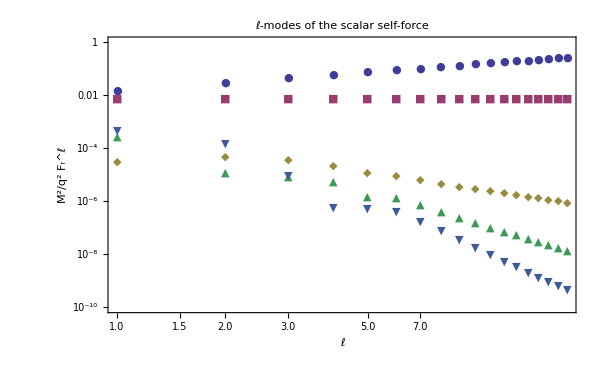

```mathematica
ListLogLogPlot[Abs@{FrRet,FrRet-Frl[-1],FrRet-Frl[-1]-Frl[0],FrRet-Frl[-1]-Frl[0]-Frl[2],FrRet-Frl[-1]-Frl[0]-Frl[2]-Frl[4]},PlotRange->{10^-10,1},DataRange->{0,18},PlotMarkers->{Automatic,Medium},Frame->True,FrameLabel->{"ℓ","M^2/q^2 F_r^ℓ"},FrameStyle->16,ImageSize->600,PlotLabel->Style["ℓ-modes of the scalar self-force",16]]
```